# H_2 dynamics

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory["~/vqe/subrecompilation"];
CreateLocalQuESTEnv["quest_link_gpu"];
```

## modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->a Subscript[Id, 0]};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]

GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace;
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]

SetAttributes[CompileMe,HoldAll]
CompileMe[nq_,matrix_,conf_,printmatrices_:False]:=Module[{ψ,ψinit,dist,cost,globalphase},
{runtime,{costlist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[CJRecompile[nq,matrix,conf]];
Print[{ansatz,θvars,aborted,fev,ncycle,"{merged, θsmall, metric, bruteforce}=",elim,finmsg}];
(*
Print[ListPlot[costlist,PlotRange->All,Joined->True,PlotMarkers->{Automatic,None},PlotLegends->{"<E>","Ground state"}]];
*)
Print[DrawCircuit[ansatz,nq]];
Print["cost=",Last@costlist,"; ngates=",Length@ansatz];
Print["runtime= ",runtime/60," minutes"];

(*sanity check*)
{ψ,ψinit}=CreateQuregs[conf["nqubit"],2];
PrepareInitState[conf,InitZeroState@ψinit];
ApplyCircuit[CloneQureg[ψ,ψinit],{Subscript[U, Sequence@Range[0,conf["nqubit"]-1]][KroneckerProduct[IdentityMatrix[2^conf["nqancilla"]],matrix]]}];
ApplyCircuit[ψ,ansatz/.CustomGatesDefinitions/.θvars];
cost=CostFidelity[ψ,ψinit];
If[(cost-Last@costlist)>10^-13,
Print["WARNIG:didn't pass sanity check"];
Print["error=",cost-Last@costlist]
];
DestroyAllQuregs[];

vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.CustomGatesDefinitions/.θvars,nq];
{dist,globalphase}=MatrixDist[matrix,vmat,conf["subspace"]];
Print["cost=",cost, " ;dist=",dist, "; globalphase=",globalphase];
If[printmatrices,
Print@MatrixForm@Chop@GetSubMatrix[matrix,conf["subspace"]];
Print@MatrixForm@Chop@GetSubMatrix[Exp[ⅈ*globalphase]vmat,conf["subspace"]];
];
{cost,dist,Length@ansatz,runtime/60,ansatz,θvars,cycleres,fev}
]
```

```mathematica
BlockByOccupation::usage="BlockByOccupation[nqubits, occupation_number], return a block that has the correct occupation number";
BlockByOccupation[nqubits_,occnum_]:=Select[Range[0,2^nqubits-1],DigitCount[#,2,1]==occnum&]
```

```mathematica
BlockBySpin::usage="BlockBySpin[spin_hamiltonian, expected_spin, nqubits], return a block that has the correct occupation number";
BlockBySpin[spinham_,spin_,nqubits_]:=Module[{ψ,ψwork,blocks,circ,j},
{ψ,ψwork}=CreateQuregs[nqubits,2];
blocks=Table[
blocks=(Reverse@Flatten@Position[Reverse@IntegerDigits[i,2,nqubits],1]-1 )/.j_Integer->Subscript[X, j];
If[Length@circ>0,ApplyCircuit[InitZeroState@ψ,circ]];
If[Abs[CalcExpecPauliSum[ψ,spinham,ψwork]-spin]≤10^-13,i,{}]
,{i,0,2^nqubits-1}];
DestroyQureg[ψ];
DestroyQureg[ψwork];
Flatten@blocks
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/H2.txt"]
```

{-0.0970663 Id_0-0.0453026 X_2 X_3 Y_0 Y_1+0.0453026 X_0 X_3 Y_1 Y_2+0.0453026 X_1 X_2 Y_0 Y_3-0.0453026 X_0 X_1 Y_2 Y_3+0.171413 Z_0+0.171413 Z_1+0.168689 Z_0 Z_1-0.223432 Z_2+0.120625 Z_0 Z_2+0.165928 Z_1 Z_2-0.223432 Z_3+0.165928 Z_0 Z_3+0.120625 Z_1 Z_3+0.174413 Z_2 Z_3,15,4}

```mathematica
{spin,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/spin.txt"];
```

```mathematica
hammat=CalcPauliSumMatrix@hamiltonian;
```

## Dynamics on various T

Subspace of interest

```mathematica
BlockByOccupation[nqubits,2]
```

{3,5,6,9,10,12}

```mathematica
BlockBySpin[spin,0,nqubits]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

### Subspace compilation: {0.001,0.01,0.1,1,4}

```mathematica
ressubH2=<||>;
DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→50,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→0.001,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

{{Rx_3[θ_8],C_2[Rz_3[θ_16]],Rx_3[θ_26],C_0[Rz_3[θ_31]],C_3[Rz_1[θ_33]],C_1[Rz_2[θ_34]],C_0[Rz_1[θ_38]],Rz_1[θ_45]},<|θ_8→0.00154887,θ_16→-0.232746,θ_26→-0.00155846,θ_31→0.233532,θ_33→0.233399,θ_34→0.000497306,θ_38→0.466841,θ_45→-0.350486|>,{},393,1,{merged, θsmall, metric, bruteforce}=,{1,37,1,3},Circuit within target precision is found}

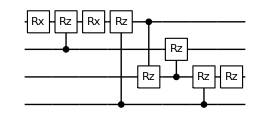

cost=9.55291×10^-8; ngates=8

runtime= 0.39558 minutes

cost=9.55291×10^-8 ;dist=0.00037415; globalphase=6.22516

{{C_0[Ry_1[θ_5]],C_3[Ry_1[θ_9]],C_2[Rz_0[θ_39]],C_3[Rx_1[θ_14]],C_3[Ry_1[θ_16]],C_3[Rx_1[θ_19]],Rz_1[θ_24],Ry_1[θ_27],C_0[Ry_1[θ_42]],Ry_1[θ_43],C_1[Rz_2[θ_46]],C_3[Rz_2[θ_48]],C_2[Rz_1[θ_49]]},<|θ_5→0.00172769,θ_9→0.0833267,θ_14→0.737493,θ_16→-0.112382,θ_19→-0.734315,θ_24→-0.11284,θ_27→-0.432848,θ_39→-0.00151477,θ_42→-0.00172795,θ_43→0.43286,θ_46→-0.0742521,θ_48→0.0743988,θ_49→0.14859|>,{},284,1,{merged, θsmall, metric, bruteforce}=,{0,27,10,0},Circuit within target precision is found}

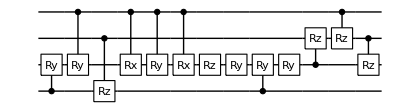

cost=2.70193×10^-8; ngates=13

runtime= 0.141817 minutes

cost=2.70193×10^-8 ;dist=0.000207401; globalphase=6.26503

{{C_2[Rz_3[θ_22]],C_3[Rz_1[θ_7]],C_2[Rz_0[θ_23]],C_3[Rz_2[θ_41]],Rz_2[θ_27],C_3[Rz_2[θ_38]],C_1[Rz_3[θ_5]],Rz_1[θ_21],C_2[Rz_3[θ_47]],C_3[Rz_1[θ_29]],C_0[Rz_1[θ_24]],C_2[Rz_1[θ_35]]},<|θ_5→-0.254547,θ_7→2.34302,θ_21→1.66761,θ_22→-0.393205,θ_23→0.716609,θ_24→-2.24308,θ_27→-0.297888,θ_29→-2.76206,θ_35→0.0434395,θ_38→-1.15067,θ_41→2.46456,θ_47→1.36585|>,{},268,1,{merged, θsmall, metric, bruteforce}=,{1,30,7,0},Circuit within target precision is found}

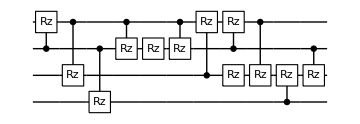

cost=2.23691×10^-8; ngates=12

runtime= 0.207045 minutes

cost=2.23691×10^-8 ;dist=0.000187423; globalphase=6.27277

{{C_1[Rz_2[θ_14]],C_2[Rz_3[θ_43]]},<|θ_14→0.000699384,θ_43→0.000932033|>,{},367,1,{merged, θsmall, metric, bruteforce}=,{0,40,6,2},Circuit within target precision is found}

-Graphics-

cost=8.45235×10^-8; ngates=2

runtime= 0.269932 minutes

cost=8.45235×10^-8 ;dist=0.000422652; globalphase=0.000385233

{{C_1[Rz_3[θ_6]],C_3[Rz_2[θ_10]],C_1[Rz_0[θ_15]],C_0[Rz_2[θ_17]],C_3[Rz_0[θ_19]],C_1[Rz_2[θ_25]],C_1[Rz_0[θ_27]],C_0[Rz_1[θ_35]],C_1[Rz_0[θ_38]],C_3[Rz_1[θ_40]],C_1[Rz_2[θ_45]],C_2[Rz_0[θ_50]]},<|θ_6→-0.437445,θ_10→0.378373,θ_15→0.166796,θ_17→0.221286,θ_19→0.453159,θ_25→-0.147836,θ_27→0.12786,θ_35→0.351549,θ_38→-1.60923,θ_40→-0.790937,θ_45→-0.889619,θ_50→0.422053|>,{},293,1,{merged, θsmall, metric, bruteforce}=,{0,36,2,0},Circuit within target precision is found}

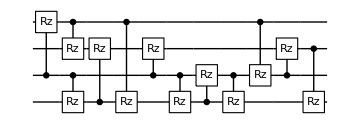

cost=3.82696×10^-8; ngates=12

runtime= 0.203215 minutes

cost=3.82696×10^-8 ;dist=0.000303322; globalphase=0.146601

{{C_3[Rz_2[θ_40]],C_1[Rz_3[θ_32]],C_3[Rz_0[θ_47]],C_2[Rx_0[θ_6]],C_2[Rx_0[θ_18]],C_1[Rz_2[θ_8]],C_0[Rz_2[θ_49]],C_0[Rz_1[θ_42]]},<|θ_6→3.14159,θ_8→-0.224716,θ_18→-3.14159,θ_32→-0.676227,θ_40→-0.22451,θ_42→-0.677956,θ_47→-0.677713,θ_49→-0.226893|>,{},388,1,{merged, θsmall, metric, bruteforce}=,{0,32,10,0},Circuit within target precision is found}

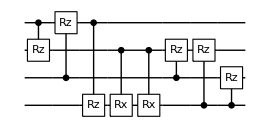

cost=3.0284×10^-8; ngates=8

runtime= 0.239182 minutes

cost=3.0284×10^-8 ;dist=0.000218257; globalphase=0.226105

{{C_1[Rz_2[θ_2]],C_1[Rz_0[θ_4]],Rz_1[θ_21],Rz_0[θ_33],C_3[Rz_1[θ_24]],C_1[Rz_3[θ_30]],C_1[Rz_0[θ_42]],C_2[Rz_1[θ_43]],C_3[Rz_0[θ_50]]},<|θ_2→2.94389,θ_4→0.967962,θ_21→2.58446,θ_24→-1.4642,θ_30→2.94386,θ_33→1.08184,θ_42→0.512103,θ_43→-0.762431,θ_50→-0.701438|>,{},324,1,{merged, θsmall, metric, bruteforce}=,{2,35,4,0},Circuit within target precision is found}

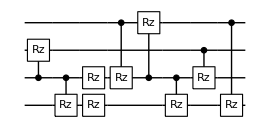

cost=2.19227×10^-8; ngates=9

runtime= 0.234237 minutes

cost=2.19227×10^-8 ;dist=0.000181707; globalphase=5.91361

{{Rz_1[θ_40],C_1[Rz_2[θ_46]],C_3[Rz_1[θ_23]],C_1[Rz_0[θ_7]],C_1[Rz_2[θ_11]],C_2[Rz_1[θ_15]]},<|θ_7→-0.00123536,θ_11→-0.487818,θ_15→-0.00168985,θ_23→-0.00154953,θ_40→0.000976622,θ_46→0.488036|>,{},351,1,{merged, θsmall, metric, bruteforce}=,{0,41,3,0},Circuit within target precision is found}

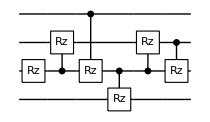

cost=3.11542×10^-8; ngates=6

runtime= 0.218956 minutes

cost=3.11542×10^-8 ;dist=0.000245539; globalphase=0.000737385

{{C_0[Rz_2[θ_17]],Rz_0[θ_38],C_0[Rz_1[θ_44]],C_2[Rz_0[θ_21]],C_0[Rz_3[θ_33]],C_0[Rz_1[θ_24]],C_3[Rz_0[θ_19]]},<|θ_17→-0.0554881,θ_19→-0.00183702,θ_21→-0.00174899,θ_24→-0.74998,θ_33→-0.0552678,θ_38→-0.0266078,θ_44→0.693183|>,{},306,1,{merged, θsmall, metric, bruteforce}=,{0,34,6,2},Circuit within target precision is found}

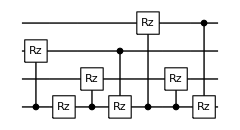

cost=2.94296×10^-8; ngates=7

runtime= 0.174155 minutes

cost=2.94296×10^-8 ;dist=0.000259209; globalphase=0.0146519

{{C_1[Rz_3[θ_13]],C_0[Rz_2[θ_21]],Rz_2[θ_25]},<|θ_13→0.00117034,θ_21→-0.00117723,θ_25→0.0015176|>,{},317,1,{merged, θsmall, metric, bruteforce}=,{1,37,8,1},Circuit within target precision is found}

-Graphics-

cost=4.99707×10^-8; ngates=3

runtime= 0.26575 minutes

cost=4.99707×10^-8 ;dist=0.000299726; globalphase=0.000401232

Cycle1, @Thu 17 Mar 2022 17:22:15, fev:384, <E>: 2.219159338401333e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 34, 6, 4, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:22:25, fev:471, <E>: 2.219159338401333e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 34, 6, 4, 0}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:22:38, fev:566, <E>: 2.219159338401333e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 34, 6, 4, 0}

pruning exceeds the maxcost: 1.×10^-7; cost=2.21916×10^-6

{{C_1[Rz_3[θ_12]],Rz_1[θ_16],C_3[Rz_2[θ_20]],C_2[Rz_0[θ_21]],C_3[Rz_1[θ_36]],C_1[Rz_2[θ_41]]},<|θ_12→1.10397,θ_16→1.36627,θ_20→0.551707,θ_21→1.08818,θ_36→-1.64444,θ_41→0.551626|>,{2,3},623,3,{merged, θsmall, metric, bruteforce}=,{0,34,6,4},Compilation is either converging or stuck. }

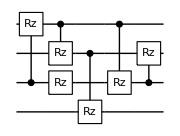

cost=2.21916×10^-6; ngates=6

runtime= 0.819958 minutes

cost=2.21916×10^-6 ;dist=0.00191119; globalphase=6.14964

Cycle1, @Thu 17 Mar 2022 17:23:00, fev:340, <E>: 2.252679278225145e-6 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 29, 10, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:23:13, fev:443, <E>: 2.252679278225145e-6 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 29, 10, 0, 0}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:23:26, fev:541, <E>: 2.252679278225145e-6 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 29, 10, 0, 0}

pruning exceeds the maxcost: 1.×10^-7; cost=2.25268×10^-6

{{C_2[Rz_3[θ_3]],C_3[Rz_1[θ_9]],C_0[Ry_1[θ_17]],Rz_3[θ_22],C_0[Rx_1[θ_20]],C_0[Rz_3[θ_23]],C_0[Ry_1[θ_26]],C_3[Rz_0[θ_33]],C_0[Rz_1[θ_35]],C_0[Ry_1[θ_43]],C_0[Rx_1[θ_49]]},<|θ_3→0.837351,θ_9→0.408933,θ_17→-0.491821,θ_20→0.773073,θ_22→-0.632363,θ_23→0.427988,θ_26→-0.92526,θ_33→-0.0156421,θ_35→0.715091,θ_43→1.56128,θ_49→-1.37829|>,{2,3},608,3,{merged, θsmall, metric, bruteforce}=,{0,29,10,0},Compilation is either converging or stuck. }

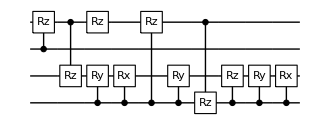

cost=2.25268×10^-6; ngates=11

runtime= 0.745809 minutes

cost=2.25268×10^-6 ;dist=0.00189845; globalphase=6.18433

Cycle1, @Thu 17 Mar 2022 17:23:57, fev:407, <E>: 2.287770642039888e-6 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:24:11, fev:514, <E>: 2.287770642039888e-6 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:24:31, fev:635, <E>: 2.287770642039888e-6 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 3}

pruning exceeds the maxcost: 1.×10^-7; cost=2.28777×10^-6

{{C_1[Rz_3[θ_39]],C_0[Rz_2[θ_12]],Rz_3[θ_47],Rx_2[θ_24],C_1[Rx_2[θ_14]],C_3[Rx_0[θ_22]],C_1[Rx_2[θ_41]],C_3[Rx_0[θ_33]],Rx_2[θ_46],C_0[Rz_3[θ_7]],C_1[Ry_2[θ_17]],C_1[Ry_2[θ_23]]},<|θ_7→0.000845273,θ_12→0.0157245,θ_14→0.176964,θ_17→0.0157009,θ_22→-0.347687,θ_23→-0.0157009,θ_24→-0.138606,θ_33→0.347687,θ_39→-0.0185005,θ_41→-0.176964,θ_46→0.138606,θ_47→0.0165718|>,{2,3},677,3,{merged, θsmall, metric, bruteforce}=,{0,38,0,0},Compilation is either converging or stuck. }

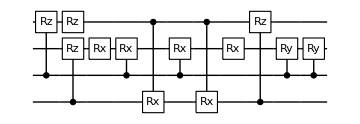

cost=2.28777×10^-6; ngates=12

runtime= 1.04481 minutes

cost=2.28777×10^-6 ;dist=0.00213756; globalphase=0.00407644

Cycle1, @Thu 17 Mar 2022 17:24:52, fev:361, <E>: 2.285304745885952e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {1, 34, 9, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:25:02, fev:449, <E>: 2.285304745885952e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {1, 34, 9, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:25:15, fev:546, <E>: 2.285304745885952e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {1, 34, 9, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=2.2853×10^-6

{{C_3[Rz_2[θ_5]],C_1[Rz_2[θ_10]],C_0[Rz_3[θ_35]],C_1[Rz_0[θ_46]],C_3[Rz_2[θ_48]],Rz_0[θ_49]},<|θ_5→-0.448799,θ_10→-0.0117249,θ_35→0.0157658,θ_46→-0.0230129,θ_48→0.476295,θ_49→0.0120868|>,{2,3},580,3,{merged, θsmall, metric, bruteforce}=,{1,34,9,0},Compilation is either converging or stuck. }

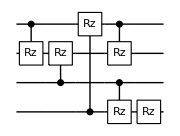

cost=2.2853×10^-6; ngates=6

runtime= 0.730855 minutes

cost=2.2853×10^-6 ;dist=0.00183786; globalphase=0.00338205

Cycle1, @Thu 17 Mar 2022 17:25:58, fev:827, <E>: 2.2605295622035726e-6 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 38, 2, 0, 6}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:26:10, fev:919, <E>: 2.2605295622035726e-6 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 38, 2, 0, 8}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:26:25, fev:1020, <E>: 2.2605295622035726e-6 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 38, 2, 0, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=2.26053×10^-6

{{C_1[Rz_0[θ_28]],Ry_0[θ_38],C_1[Rz_2[θ_2]],C_0[Rz_3[θ_9]],Rx_0[θ_16],C_3[Rz_1[θ_27]],Ry_0[θ_47],Rz_0[θ_44],C_3[Rx_0[θ_23]]},<|θ_2→0.319683,θ_9→0.319316,θ_16→-1.79279,θ_23→0.318959,θ_27→0.304414,θ_28→0.30852,θ_38→1.60629,θ_44→1.79347,θ_47→-1.40727|>,{2,3},1119,3,{merged, θsmall, metric, bruteforce}=,{0,38,2,0},Compilation is either converging or stuck. }

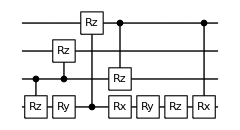

cost=2.26053×10^-6; ngates=9

runtime= 1.13548 minutes

cost=2.26053×10^-6 ;dist=0.00188107; globalphase=6.21046

Cycle1, @Thu 17 Mar 2022 17:26:50, fev:317, <E>: 2.190224275611108e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:27:00, fev:408, <E>: 2.190224275611108e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:27:13, fev:501, <E>: 2.190224275611108e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 3}

I'm slowing down. Number of gates is increased to 70 @cycle 4

Cycle4, @Thu 17 Mar 2022 17:27:32, fev:607, <E>: 2.190224275611108e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.19022×10^-6

{{Rz_0[θ_6],C_1[Rz_0[θ_12]],C_0[Rz_2[θ_32]],C_1[Rz_2[θ_34]],C_2[Rz_3[θ_43]],C_3[Rz_2[θ_45]]},<|θ_6→0.24609,θ_12→-0.492061,θ_32→-0.155974,θ_34→-0.152443,θ_43→0.015843,θ_45→0.324237|>,{2,3,4},645,4,{merged, θsmall, metric, bruteforce}=,{0,39,5,0},I keep failing to lower the energy. }

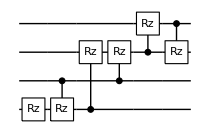

cost=2.19022×10^-6; ngates=6

runtime= 1.05732 minutes

cost=2.19022×10^-6 ;dist=0.00181541; globalphase=0.0423764

Cycle1, @Thu 17 Mar 2022 17:27:58, fev:380, <E>: 2.1891668916529383e-6 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 33, 7, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:28:07, fev:451, <E>: 2.1891668916529383e-6 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 33, 7, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:28:19, fev:542, <E>: 2.1891668916529383e-6 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 33, 7, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.18917×10^-6

{{C_2[Rz_3[θ_11]],C_3[Rz_1[θ_15]],C_3[Rz_2[θ_16]],C_1[Rz_2[θ_18]],Rz_3[θ_28],C_0[Rz_2[θ_25]],C_2[Rz_1[θ_27]],C_0[Rz_3[θ_33]],Rz_1[θ_45],C_0[Rz_1[θ_46]]},<|θ_11→-0.814644,θ_15→3.32646,θ_16→0.648351,θ_18→0.675455,θ_25→-1.30803,θ_27→-0.143605,θ_28→-0.329878,θ_33→1.4902,θ_45→-2.68583,θ_46→2.18879|>,{2,3},598,3,{merged, θsmall, metric, bruteforce}=,{0,33,7,0},I keep failing to lower the energy. }

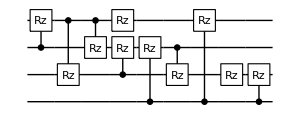

cost=2.18917×10^-6; ngates=10

runtime= 0.775845 minutes

cost=2.18917×10^-6 ;dist=0.00181218; globalphase=5.78196

Cycle1, @Thu 17 Mar 2022 17:28:50, fev:503, <E>: 2.257953953033187e-6 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 37, 0, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:28:59, fev:603, <E>: 2.257953953033187e-6 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 37, 0, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:29:15, fev:708, <E>: 2.257953953033187e-6 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 37, 0, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=2.25795×10^-6

{{C_2[Rx_3[θ_1]],C_2[Rz_1[θ_2]],C_0[Rz_1[θ_3]],C_2[Rx_3[θ_6]],C_3[Rz_0[θ_9]],C_1[Rx_3[θ_13]],Rz_0[θ_43],C_1[Rx_3[θ_17]],Rz_3[θ_32],C_1[Ry_2[θ_20]],C_1[Ry_2[θ_26]],C_2[Rz_3[θ_33]],C_2[Rz_1[θ_37]]},<|θ_1→0.174431,θ_2→-0.261779,θ_3→0.665155,θ_6→-0.174431,θ_9→0.68317,θ_13→0.213815,θ_17→-0.213815,θ_20→-0.0638022,θ_26→0.0638022,θ_32→0.330822,θ_33→-0.661779,θ_37→-0.418447,θ_43→-0.349551|>,{2,3},782,3,{merged, θsmall, metric, bruteforce}=,{0,37,0,0},Compilation is either converging or stuck. }

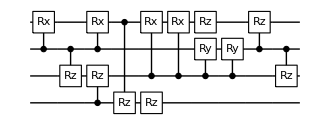

cost=2.25795×10^-6; ngates=13

runtime= 0.905239 minutes

cost=2.25795×10^-6 ;dist=0.00182935; globalphase=0.00338725

Cycle1, @Thu 17 Mar 2022 17:29:38, fev:339, <E>: 2.220287058429804e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:29:47, fev:419, <E>: 2.220287058429804e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:30:02, fev:525, <E>: 2.220287058429804e-6 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 0, 5}

pruning exceeds the maxcost: 1.×10^-7; cost=2.22029×10^-6

{{C_3[Rz_0[θ_15]],C_2[Rz_3[θ_26]],Rz_0[θ_27],C_0[Rz_3[θ_31]],C_3[Rz_2[θ_36]],C_1[Rz_3[θ_45]]},<|θ_15→-0.307312,θ_26→-0.106196,θ_27→0.153994,θ_31→0.216445,θ_36→0.0157577,θ_45→-0.0945056|>,{2,3},568,3,{merged, θsmall, metric, bruteforce}=,{0,38,6,0},Compilation is either converging or stuck. }

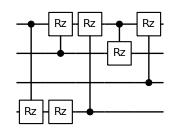

cost=2.22029×10^-6; ngates=6

runtime= 0.721765 minutes

cost=2.22029×10^-6 ;dist=0.00182625; globalphase=0.0270084

Cycle1, @Thu 17 Mar 2022 17:30:33, fev:365, <E>: 2.1892114522303885e-6 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 23, 0, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:30:48, fev:468, <E>: 2.1892114522303885e-6 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 23, 0, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:31:08, fev:581, <E>: 2.1892114522303885e-6 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 23, 0, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=2.18921×10^-6

{{Rz_2[θ_22],C_3[Rz_0[θ_30]],C_3[Rz_1[θ_44]],C_1[Rx_2[θ_47]],C_3[Rz_1[θ_45]],C_0[Rz_1[θ_38]],C_1[Rx_2[θ_43]],C_0[Rz_3[θ_12]],C_3[Ry_0[θ_21]],Rz_2[θ_28],C_3[Rx_0[θ_40]],C_3[Rz_0[θ_7]],C_2[Rz_3[θ_6]],Rz_0[θ_11],Rz_2[θ_17],C_1[Rz_3[θ_32]],C_3[Rx_0[θ_19]],Rz_1[θ_31],C_3[Ry_0[θ_41]],C_0[Rz_2[θ_33]],C_3[Rz_0[θ_20]],C_1[Rz_2[θ_42]],C_2[Rz_1[θ_26]],C_2[Rx_1[θ_1]],C_2[Rz_3[θ_25]],C_2[Rx_1[θ_39]],C_0[Rz_2[θ_46]]},<|θ_1→0.268545,θ_6→-0.767713,θ_7→0.881704,θ_11→-0.447613,θ_12→0.751498,θ_17→1.1235,θ_19→-0.672888,θ_20→0.495462,θ_21→-1.19573,θ_22→-0.309477,θ_25→0.938765,θ_26→-0.628376,θ_28→0.144958,θ_30→-0.214418,θ_31→0.67647,θ_32→0.0416357,θ_33→0.521697,θ_38→0.313619,θ_39→-0.268545,θ_40→-0.365091,θ_41→1.11793,θ_42→-1.48252,θ_43→0.203932,θ_44→0.272458,θ_45→-0.362249,θ_46→0.00705567,θ_47→-0.203932|>,{2,3},681,3,{merged, θsmall, metric, bruteforce}=,{0,23,0,0},I keep failing to lower the energy. }

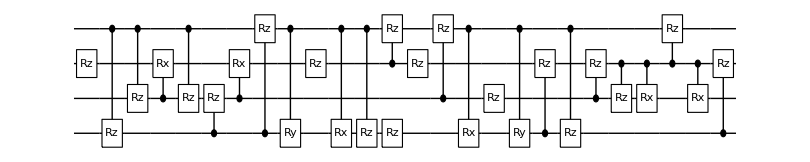

cost=2.18921×10^-6; ngates=27

runtime= 1.13589 minutes

cost=2.18921×10^-6 ;dist=0.00181223; globalphase=6.16642

Cycle1, @Thu 17 Mar 2022 17:31:33, fev:376, <E>: 0.0002187228542664954 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 30, 6, 1, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:31:45, fev:467, <E>: 0.0002187228542664954 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 30, 6, 1, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:32:04, fev:598, <E>: 0.0002187228542664954 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 30, 6, 1, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218723

{{Rz_1[θ_11],C_2[Rx_3[θ_4]],C_0[Rz_1[θ_12]],Rx_3[θ_8],C_2[Rx_3[θ_21]],Rx_3[θ_40],C_2[Rx_1[θ_23]],C_2[Rx_0[θ_26]],C_2[Ry_0[θ_34]],Rz_0[θ_36],C_2[Rx_0[θ_37]],C_2[Rx_1[θ_45]]},<|θ_4→1.51389,θ_8→-0.224562,θ_11→-0.0814942,θ_12→0.00508521,θ_21→-1.51389,θ_23→0.086205,θ_26→0.896717,θ_34→0.0755909,θ_36→-0.0604876,θ_37→-0.899018,θ_40→0.224562,θ_45→-0.086205|>,{2,3},657,3,{merged, θsmall, metric, bruteforce}=,{1,30,6,1},Compilation is either converging or stuck. }

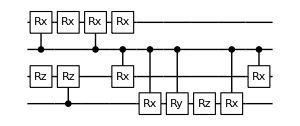

cost=0.000218723; ngates=12

runtime= 0.905943 minutes

cost=0.000218723 ;dist=0.018259; globalphase=0.0428947

Cycle1, @Thu 17 Mar 2022 17:32:22, fev:440, <E>: 0.00021867004807063495 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:32:34, fev:544, <E>: 0.00021867004807063495 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 4}

Cycle3, @Thu 17 Mar 2022 17:33:15, fev:1082, <E>: 3.106614465342439e-6 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 75, 7, 0, 5}

{{C_1[Rz_3[θ_112]],C_3[Rx_1[θ_139]],C_0[Rz_1[θ_144]],C_0[Rx_3[θ_102]],Rz_1[θ_123],C_2[Rx_0[θ_54]],Ry_3[θ_84],C_1[Ry_2[θ_76]],C_2[Rx_3[θ_145]],Ry_3[θ_82],C_2[Rz_0[θ_50]],C_2[Ry_0[θ_115]],C_0[Ry_3[θ_87]],C_0[Rz_3[θ_142]],C_3[Rx_1[θ_17]]},<|θ_17→-3.14159,θ_50→9.4745,θ_54→3.14159,θ_76→-0.036365,θ_82→1.5708,θ_84→-1.5708,θ_87→-3.14159,θ_102→3.14159,θ_112→0.0633632,θ_115→-3.14159,θ_123→-3.06046,θ_139→3.14159,θ_142→-3.09673,θ_144→6.17536,θ_145→-0.0493339|>,{2},1879,4,{merged, θsmall, metric, bruteforce}=,{0,120,10,0},Circuit within target precision is found}

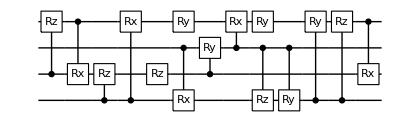

cost=8.91554×10^-8; ngates=15

runtime= 1.89256 minutes

cost=8.91554×10^-8 ;dist=0.000408202; globalphase=1.61483

Cycle1, @Thu 17 Mar 2022 17:35:44, fev:2159, <E>: 0.00021870683994795748 nansatz:19 merged-smallθ,metric,bf,gmerged: {1, 30, 0, 0, 2}

Cycle2, @Thu 17 Mar 2022 17:36:18, fev:2731, <E>: 0.00007336003195113072 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 74, 3, 0, 4}

{{Rz_1[θ_52],C_2[Rz_0[θ_93]],C_1[Ry_0[θ_64]],C_2[Ry_1[θ_72]],C_2[Rx_3[θ_73]],Rx_2[θ_74],C_3[Rz_2[θ_113]],Rz_3[θ_6],C_1[Rx_2[θ_121]],C_3[Rx_2[θ_112]],C_0[Ry_2[θ_123]],C_2[Ry_1[θ_76]],C_1[Ry_0[θ_80]],C_1[Rz_2[θ_86]],C_0[Rz_3[θ_125]],C_2[Ry_3[θ_8]],Rz_0[θ_32],C_2[Rz_0[θ_95]]},<|θ_6→2.03972,θ_8→3.14159,θ_32→2.54698,θ_52→2.05918,θ_64→-3.14159,θ_72→3.14159,θ_73→3.14159,θ_74→0.0726147,θ_76→-3.14159,θ_80→3.14159,θ_86→-1.01091,θ_93→-1.15506,θ_95→0.108464,θ_112→0.00121169,θ_113→-1.06509,θ_121→-0.0363576,θ_123→0.063484,θ_125→0.0679463|>,{},3623,3,{merged, θsmall, metric, bruteforce}=,{1,104,7,0},Circuit within target precision is found}

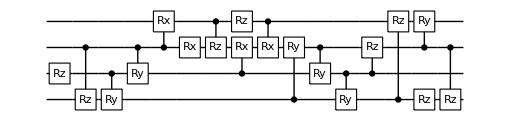

cost=6.29021×10^-8; ngates=18

runtime= 3.00464 minutes

cost=6.29021×10^-8 ;dist=0.000394984; globalphase=1.86622

Cycle1, @Thu 17 Mar 2022 17:37:22, fev:301, <E>: 0.000218696089971826 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 35, 8, 1, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:37:32, fev:388, <E>: 0.000218696089971826 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 35, 8, 1, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:37:43, fev:498, <E>: 0.000218696089971826 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 35, 8, 1, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218696

{{C_3[Ry_1[θ_32]],C_3[Rz_2[θ_17]],C_0[Rz_1[θ_15]],C_3[Ry_1[θ_19]],C_0[Rz_3[θ_11]],C_2[Rz_3[θ_3]]},<|θ_3→0.0414511,θ_11→0.116101,θ_15→-0.0793072,θ_17→0.078619,θ_19→3.14015,θ_32→-3.14016|>,{2,3},531,3,{merged, θsmall, metric, bruteforce}=,{0,35,8,1},Compilation is either converging or stuck. }

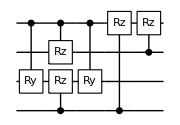

cost=0.000218696; ngates=6

runtime= 0.646516 minutes

cost=0.000218696 ;dist=0.018244; globalphase=0.0140143

Cycle1, @Thu 17 Mar 2022 17:37:57, fev:332, <E>: 0.00021876228724893032 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 35, 7, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:38:06, fev:423, <E>: 0.00021876228724893032 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 35, 7, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:38:20, fev:517, <E>: 0.00021876228724893032 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 35, 7, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218762

{{C_3[Rz_1[θ_31]],C_2[Ry_3[θ_39]],C_2[Rz_0[θ_21]],C_2[Ry_3[θ_11]],C_1[Rz_2[θ_14]],Rz_1[θ_40],C_3[Rz_2[θ_37]],C_2[Ry_3[θ_23]]},<|θ_11→-0.0243559,θ_14→-0.00213148,θ_21→-0.157082,θ_23→-0.00164413,θ_31→0.118004,θ_37→0.00236687,θ_39→0.0260007,θ_40→-0.137442|>,{2,3},542,3,{merged, θsmall, metric, bruteforce}=,{0,35,7,0},Compilation is either converging or stuck. }

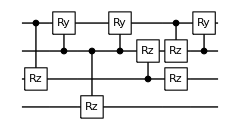

cost=0.000218762; ngates=8

runtime= 0.588935 minutes

cost=0.000218762 ;dist=0.0181211; globalphase=0.0436012

Cycle1, @Thu 17 Mar 2022 17:38:35, fev:463, <E>: 0.00021875676474414352 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 28, 12, 2, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:38:46, fev:562, <E>: 0.00021875676474414352 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 28, 12, 2, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:39:01, fev:663, <E>: 0.00021875676474414352 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 28, 12, 2, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218757

{{C_0[Ry_2[θ_21]],C_0[Rx_2[θ_32]],C_0[Ry_2[θ_45]],C_2[Rz_1[θ_40]],Rz_0[θ_5],Rz_2[θ_11],C_1[Rz_3[θ_9]],C_2[Rz_1[θ_20]]},<|θ_5→-0.00268123,θ_9→0.151626,θ_11→0.172437,θ_20→-0.118161,θ_21→-1.5708,θ_32→0.192799,θ_40→0.112974,θ_45→1.5708|>,{2,3},706,3,{merged, θsmall, metric, bruteforce}=,{0,28,12,2},Compilation is either converging or stuck. }

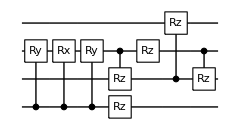

cost=0.000218757; ngates=8

runtime= 0.660275 minutes

cost=0.000218757 ;dist=0.0182862; globalphase=0.0441175

Cycle1, @Thu 17 Mar 2022 17:39:29, fev:594, <E>: 0.00021875156703365928 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 35, 6, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:39:42, fev:694, <E>: 0.00021875156703365928 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 35, 6, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:39:58, fev:797, <E>: 0.00021875156703365928 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 35, 6, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218752

{{C_3[Rx_0[θ_3]],C_1[Rz_2[θ_26]],C_1[Rz_3[θ_1]],C_3[Ry_0[θ_5]],C_1[Rz_2[θ_11]],C_3[Rx_0[θ_43]],Rz_3[θ_27],C_0[Rz_1[θ_15]],C_2[Rz_3[θ_16]]},<|θ_1→0.422332,θ_3→1.57004,θ_5→-0.151186,θ_11→0.460465,θ_15→0.150392,θ_16→0.312683,θ_26→-0.152311,θ_27→-0.21333,θ_43→-1.57004|>,{2,3},889,3,{merged, θsmall, metric, bruteforce}=,{0,35,6,0},Compilation is either converging or stuck. }

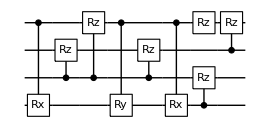

cost=0.000218752; ngates=9

runtime= 0.92211 minutes

cost=0.000218752 ;dist=0.0183039; globalphase=6.21144

Cycle1, @Thu 17 Mar 2022 17:40:32, fev:424, <E>: 0.0002186832740719291 nansatz:20 merged-smallθ,metric,bf,gmerged: {1, 28, 0, 1, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:40:49, fev:524, <E>: 0.0002186832740719291 nansatz:20 merged-smallθ,metric,bf,gmerged: {1, 28, 0, 1, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:41:07, fev:626, <E>: 0.0002186832740719291 nansatz:20 merged-smallθ,metric,bf,gmerged: {1, 28, 0, 1, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218683

{{C_3[Rz_1[θ_1]],Rz_2[θ_7],C_3[Rz_0[θ_2]],Rz_1[θ_11],C_2[Rz_0[θ_8]],C_3[Ry_1[θ_13]],C_2[Rz_3[θ_16]],C_3[Ry_1[θ_17]],C_0[Rz_2[θ_19]],C_3[Rz_2[θ_20]],Rz_0[θ_23],Rz_1[θ_25],C_2[Rz_3[θ_26]],C_2[Rz_0[θ_27]],C_0[Rz_3[θ_28]],C_2[Rz_1[θ_32]],C_0[Rz_3[θ_30]],C_2[Rz_1[θ_36]],C_3[Rz_2[θ_44]],C_2[Rz_1[θ_46]]},<|θ_1→1.15413,θ_2→0.478768,θ_7→1.33923,θ_8→0.0434298,θ_11→-0.212388,θ_13→0.127339,θ_16→1.53739,θ_17→-0.127339,θ_19→-0.389752,θ_20→-1.63648,θ_23→0.397359,θ_25→-0.23395,θ_26→0.125458,θ_27→-0.502198,θ_28→-2.45449,θ_30→1.76431,θ_32→1.39478,θ_36→-0.480635,θ_44→0.319977,θ_46→-0.360888|>,{2,3},718,3,{merged, θsmall, metric, bruteforce}=,{1,28,0,1},Compilation is either converging or stuck. }

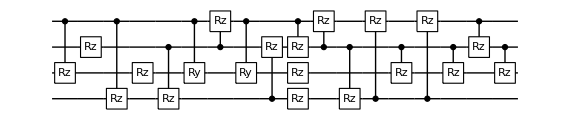

cost=0.000218683; ngates=20

runtime= 1.14601 minutes

cost=0.000218683 ;dist=0.0181212; globalphase=6.24061

Cycle1, @Thu 17 Mar 2022 17:41:44, fev:466, <E>: 0.00021877433889927467 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 1, 3}

Cycle2, @Thu 17 Mar 2022 17:42:22, fev:879, <E>: 0.00021867848742462836 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 54, 0, 1, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:42:45, fev:985, <E>: 0.00021867848742462836 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 54, 0, 1, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Thu 17 Mar 2022 17:43:07, fev:1082, <E>: 0.00021867848742462836 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 54, 0, 1, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218678

{{C_0[Rz_2[θ_1]],C_0[Rz_1[θ_2]],C_3[Rz_1[θ_3]],C_3[Rz_1[θ_9]],C_0[Rz_3[θ_10]],Rz_1[θ_35],C_3[Rz_2[θ_15]],C_0[Rz_2[θ_20]],C_3[Rz_0[θ_23]],C_3[Rx_0[θ_28]],Rz_3[θ_33],C_3[Rx_0[θ_37]],C_3[Rz_0[θ_44]],C_0[Rz_2[θ_47]],C_1[Rx_3[θ_52]],C_2[Ry_3[θ_53]],Rz_2[θ_59],C_0[Rx_3[θ_55]],C_3[Rz_1[θ_56]],C_2[Rx_3[θ_60]],C_3[Rz_1[θ_62]],C_0[Rx_3[θ_65]],C_0[Ry_3[θ_68]],C_2[Rz_0[θ_69]],C_2[Rz_3[θ_70]],Rz_0[θ_72],C_1[Rz_3[θ_71]],C_0[Rx_3[θ_73]],C_1[Rz_2[θ_81]],Rx_3[θ_77],Rz_1[θ_86],Ry_3[θ_82],C_0[Rz_3[θ_83]],C_2[Rx_3[θ_88]],C_0[Rz_3[θ_89]]},<|θ_1→0.89381,θ_2→0.0897924,θ_3→-1.07425,θ_9→-0.365661,θ_10→0.176388,θ_15→-0.406083,θ_20→0.964631,θ_23→0.516012,θ_28→-0.0836366,θ_33→-0.949944,θ_35→-0.259886,θ_37→0.0836366,θ_44→-0.595513,θ_47→-3.31004,θ_52→0.00218302,θ_53→0.000338606,θ_55→1.10006,θ_56→-0.00885819,θ_59→0.365021,θ_60→-0.0010757,θ_62→0.00720019,θ_65→-1.10093,θ_68→0.000294272,θ_69→-0.662555,θ_70→-0.771865,θ_71→2.42631,θ_72→-0.304433,θ_73→-0.00111402,θ_77→0.0018032,θ_81→-0.0657805,θ_82→-0.00114152,θ_83→-1.40528,θ_86→0.260315,θ_88→-0.00129226,θ_89→0.281453|>,{3,4},1200,4,{merged, θsmall, metric, bruteforce}=,{0,54,0,1},I keep failing to lower the energy. }

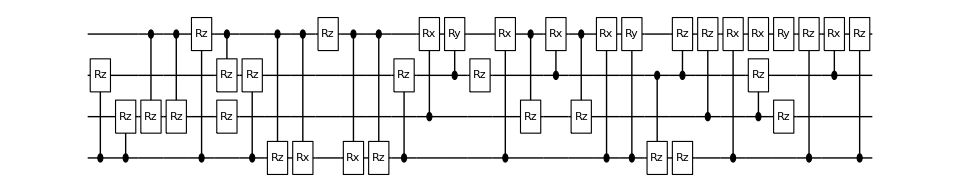

cost=0.000218678; ngates=35

runtime= 2.03929 minutes

cost=0.000218678 ;dist=0.0181275; globalphase=0.316059

Cycle1, @Thu 17 Mar 2022 17:43:34, fev:294, <E>: 0.0002186956137611995 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 27, 7, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:43:48, fev:389, <E>: 0.0002186956137611995 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 27, 7, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 17:44:06, fev:494, <E>: 0.0002186956137611995 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 27, 7, 0, 3}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218696

{{C_0[Rz_2[θ_23]],C_1[Rz_0[θ_30]],C_2[Rx_1[θ_36]],C_2[Rx_0[θ_4]],C_2[Rx_0[θ_13]],C_2[Ry_1[θ_26]],C_2[Rz_3[θ_1]],Rz_1[θ_25],C_2[Rx_1[θ_16]],C_1[Rx_3[θ_39]],Rz_2[θ_38],Rz_1[θ_33],C_2[Rz_0[θ_40]],C_3[Rz_0[θ_10]],C_1[Rx_3[θ_37]],Rz_3[θ_22]},<|θ_1→-0.307634,θ_4→-0.0114367,θ_10→-0.107651,θ_13→0.0114367,θ_16→0.295392,θ_22→0.297914,θ_23→-0.131958,θ_25→0.787206,θ_26→0.212311,θ_30→0.226974,θ_33→-0.733151,θ_36→-0.206951,θ_37→-0.00543424,θ_38→0.210077,θ_39→0.00543317,θ_40→0.0105576|>,{2,3},556,3,{merged, θsmall, metric, bruteforce}=,{0,27,7,0},Compilation is either converging or stuck. }

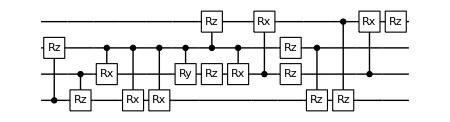

cost=0.000218696; ngates=16

runtime= 0.841356 minutes

cost=0.000218696 ;dist=0.0182023; globalphase=0.0641724

Cycle1, @Thu 17 Mar 2022 17:44:47, fev:604, <E>: 0.019627501483701626 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 24, 6, 1, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:45:00, fev:684, <E>: 0.019627501483701626 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 24, 6, 1, 4}

Cycle3, @Thu 17 Mar 2022 17:45:51, fev:1373, <E>: 0.00005728164399487756 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 74, 10, 1, 6}

Cycle4, @Thu 17 Mar 2022 17:46:24, fev:1958, <E>: 2.2357835582909047e-9 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 110, 17, 1, 11}

{{Rz_0[θ_6],C_1[Rz_3[θ_143]],C_3[Ry_1[θ_116]],C_2[Rz_1[θ_2]],C_1[Rz_3[θ_3]],C_2[Ry_0[θ_79]],C_2[Rx_3[θ_67]],C_3[Rx_1[θ_103]],C_3[Ry_2[θ_126]],C_0[Rx_2[θ_133]],C_1[Ry_2[θ_110]],C_0[Rx_2[θ_83]],C_2[Rz_3[θ_129]],C_2[Ry_0[θ_71]],C_2[Ry_3[θ_75]],C_1[Rz_2[θ_24]],C_2[Ry_1[θ_30]]},<|θ_2→-8.3749,θ_3→-9.32908,θ_6→-3.0801,θ_24→-11.7368,θ_30→3.14159,θ_67→3.14159,θ_71→-3.14163,θ_75→3.14159,θ_79→3.14154,θ_83→-8.96725,θ_103→-3.14159,θ_110→0.362319,θ_116→3.14159,θ_126→-0.362331,θ_129→-3.18653,θ_133→8.97569,θ_143→-8.73735|>,{2},2146,4,{merged, θsmall, metric, bruteforce}=,{0,110,17,1},Circuit within target precision is found}

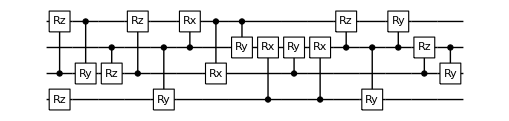

cost=2.23578×10^-9; ngates=17

runtime= 2.34237 minutes

cost=2.23578×10^-9 ;dist=0.0000615312; globalphase=1.99973

Cycle1, @Thu 17 Mar 2022 17:46:51, fev:355, <E>: 0.01962750592681084 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 40, 2, 0, 0}

Cycle2, @Thu 17 Mar 2022 17:48:23, fev:1965, <E>: 0.0027410790345029357 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 70, 2, 0, 1}

{{C_1[Rz_3[θ_8]],C_1[Rx_2[θ_22]],Ry_3[θ_129],Rz_2[θ_90],C_0[Rz_3[θ_127]],C_0[Ry_3[θ_98]],C_0[Rz_3[θ_104]],C_1[Ry_0[θ_28]],C_2[Rz_1[θ_117]],Rx_1[θ_73],C_2[Rz_1[θ_113]],C_1[Rx_3[θ_67]],C_0[Ry_1[θ_53]],C_0[Rz_1[θ_95]],C_3[Rz_0[θ_114]],C_3[Rz_1[θ_75]],C_1[Rx_2[θ_51]],Ry_3[θ_103],C_1[Ry_0[θ_47]],C_0[Rz_2[θ_89]],C_3[Rz_0[θ_126]]},<|θ_8→-4.9011,θ_22→-3.14159,θ_28→-3.14159,θ_47→3.14159,θ_51→3.14159,θ_53→0.325073,θ_67→-0.743966,θ_73→0.32536,θ_75→9.42484,θ_89→-1.78992,θ_90→5.69686,θ_95→3.34138,θ_98→2.91099,θ_103→4.71262,θ_104→-1.56894,θ_113→-1.94275,θ_114→-3.14126,θ_117→-4.93389,θ_126→2.8981,θ_127→-7.85218,θ_129→-1.57053|>,{},4070,3,{merged, θsmall, metric, bruteforce}=,{0,103,6,0},Circuit within target precision is found}

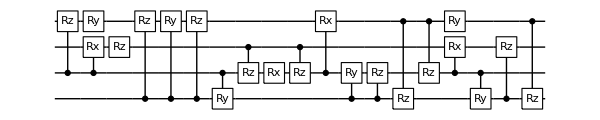

cost=1.94852×10^-8; ngates=21

runtime= 3.75492 minutes

cost=1.94852×10^-8 ;dist=0.000175845; globalphase=4.36724

Cycle1, @Thu 17 Mar 2022 17:50:42, fev:338, <E>: 0.01962749527155927 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 35, 7, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 17:50:52, fev:423, <E>: 0.01962749527155927 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 35, 7, 0, 4}

Cycle3, @Thu 17 Mar 2022 17:51:26, fev:841, <E>: 0.0000619481285080159 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 74, 10, 0, 5}

Cycle4, @Thu 17 Mar 2022 17:52:07, fev:1405, <E>: 0.00004057130759516081 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 111, 20, 0, 5}

Cycle5, @Thu 17 Mar 2022 17:53:12, fev:2542, <E>: 0.000038017812596380374 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 154, 23, 1, 6}

{{C_0[Rz_1[θ_223]],C_0[Rz_2[θ_240]],C_0[Rx_1[θ_54]],C_0[Ry_3[θ_62]],C_2[Rz_1[θ_206]],C_0[Rz_1[θ_131]],Rz_3[θ_225],C_0[Ry_2[θ_68]],C_2[Ry_0[θ_71]],C_2[Rz_3[θ_229]],C_2[Rz_1[θ_231]],C_0[Rz_3[θ_234]],C_2[Rx_0[θ_203]],C_0[Rz_3[θ_196]],C_0[Rx_1[θ_237]],Rz_1[θ_226],C_0[Ry_2[θ_84]],C_0[Ry_3[θ_148]],C_0[Rz_1[θ_150]]},<|θ_54→3.14159,θ_62→3.14159,θ_68→-3.14159,θ_71→-0.316084,θ_84→3.14159,θ_131→-2.08368,θ_148→-3.14159,θ_150→0.924588,θ_196→0.386391,θ_203→-0.139182,θ_206→-2.28877,θ_223→-0.637854,θ_225→-3.1717,θ_226→1.96739,θ_229→1.38735,θ_231→-2.28281,θ_234→0.285674,θ_237→3.14159,θ_240→1.63875|>,{2},3144,6,{merged, θsmall, metric, bruteforce}=,{0,193,23,6},Circuit within target precision is found}

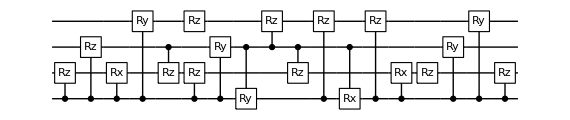

cost=1.16805×10^-8; ngates=19

runtime= 3.50688 minutes

cost=1.16805×10^-8 ;dist=0.000137514; globalphase=6.21181

Cycle1, @Thu 17 Mar 2022 17:54:43, fev:829, <E>: 0.00005689860159552307 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 33, 0, 0, 0}

Cycle2, @Thu 17 Mar 2022 17:55:20, fev:1315, <E>: 2.0506765028294183e-6 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 70, 4, 0, 4}

{{C_2[Ry_3[θ_71]],C_2[Ry_1[θ_11]],C_2[Ry_0[θ_12]],C_1[Rz_2[θ_54]],C_1[Rx_2[θ_87]],C_3[Rx_2[θ_77]],C_0[Rx_2[θ_13]],C_2[Ry_0[θ_17]],C_2[Ry_3[θ_23]],C_1[Rz_2[θ_44]],C_2[Ry_1[θ_48]],C_1[Rz_2[θ_91]],Rz_2[θ_93],C_0[Rz_1[θ_104]],C_2[Rz_3[θ_96]],Rz_2[θ_118]},<|θ_11→3.14159,θ_12→3.14159,θ_13→0.0184668,θ_17→-3.14159,θ_23→3.14159,θ_44→-1.98407,θ_48→3.14159,θ_54→7.0805,θ_71→-3.14159,θ_77→0.343954,θ_87→-0.343954,θ_91→6.6462,θ_93→5.27961,θ_96→7.87793,θ_104→-1.18676,θ_118→5.3544|>,{},2301,3,{merged, θsmall, metric, bruteforce}=,{0,107,4,3},Circuit within target precision is found}

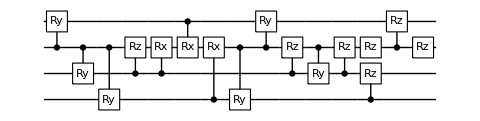

cost=1.9356×10^-8; ngates=16

runtime= 2.02684 minutes

cost=1.9356×10^-8 ;dist=0.000156083; globalphase=1.90897

Cycle1, @Thu 17 Mar 2022 17:56:19, fev:391, <E>: 0.019627596379341194 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 36, 5, 0, 0}

Cycle2, @Thu 17 Mar 2022 17:56:47, fev:811, <E>: 0.01526885600735084 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 72, 6, 0, 2}

Cycle3, @Thu 17 Mar 2022 17:57:09, fev:1133, <E>: 0.00005738586497550102 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 105, 12, 0, 2}

Cycle4, @Thu 17 Mar 2022 17:57:49, fev:1643, <E>: 0.000056869242327617364 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 131, 12, 0, 3}

{{C_0[Rx_2[θ_62]],C_1[Rz_2[θ_183]],C_0[Rz_1[θ_174]],C_3[Rx_1[θ_162]],C_3[Rz_2[θ_164]],C_0[Ry_3[θ_74]],Rz_3[θ_189],C_2[Ry_0[θ_197]],C_3[Rz_0[θ_142]],C_0[Rz_3[θ_205]],C_2[Ry_0[θ_122]],C_0[Ry_3[θ_77]],C_3[Rx_1[θ_78]],C_0[Rz_2[θ_150]],C_0[Rx_2[θ_84]],C_1[Rz_3[θ_151]]},<|θ_62→3.14159,θ_74→3.14159,θ_77→-3.14159,θ_78→-3.14159,θ_84→-3.14159,θ_122→0.33897,θ_142→-0.817307,θ_150→-0.777158,θ_151→-2.60312,θ_162→3.14159,θ_164→-0.134914,θ_174→-0.94521,θ_183→-0.338669,θ_189→1.60349,θ_197→0.0473527,θ_205→-2.21702|>,{},2639,5,{merged, θsmall, metric, bruteforce}=,{2,173,18,0},Circuit within target precision is found}

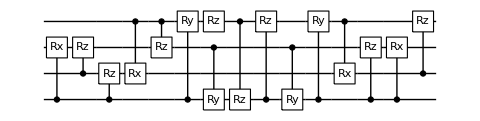

cost=9.8558×10^-9; ngates=16

runtime= 2.92523 minutes

cost=9.8558×10^-9 ;dist=0.000145437; globalphase=0.676415

Cycle1, @Thu 17 Mar 2022 17:59:24, fev:472, <E>: 0.015270478322528147 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 0, 0}

{{C_1[Rz_2[θ_51]],C_3[Ry_0[θ_7]],C_2[Rz_1[θ_57]],C_2[Rx_1[θ_16]],C_3[Ry_2[θ_60]],Ry_3[θ_66],C_2[Rz_1[θ_63]],Rz_3[θ_25],C_2[Rz_3[θ_65]],C_0[Ry_3[θ_78]],C_1[Rz_2[θ_76]],C_1[Rz_3[θ_77]],C_3[Ry_0[θ_34]],Rz_1[θ_40],C_2[Rz_0[θ_84]],C_0[Rz_2[θ_80]],C_3[Ry_2[θ_37]],C_2[Ry_1[θ_45]]},<|θ_7→3.14159,θ_16→-3.14159,θ_25→-0.949446,θ_34→-3.14159,θ_37→-3.14159,θ_40→-3.16786,θ_45→-3.14159,θ_51→-0.322554,θ_57→0.32404,θ_60→3.14159,θ_63→-1.12137,θ_65→7.23212,θ_66→0.362119,θ_76→-1.20738,θ_77→-6.60429,θ_78→-0.361507,θ_80→3.12872,θ_84→-9.41683|>,{},1637,2,{merged, θsmall, metric, bruteforce}=,{0,68,3,0},Circuit within target precision is found}

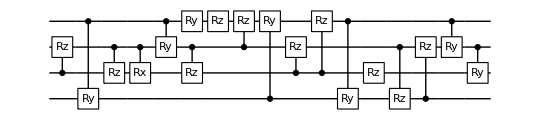

cost=8.04259×10^-8; ngates=18

runtime= 1.3406 minutes

cost=8.04259×10^-8 ;dist=0.000335744; globalphase=2.49126

Cycle1, @Thu 17 Mar 2022 18:00:45, fev:429, <E>: 0.00005698703751977341 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 35, 1, 0, 2}

{{C_3[Rx_1[θ_3]],Rz_0[θ_5],C_3[Rz_0[θ_67]],C_1[Rz_2[θ_11]],Rz_3[θ_10],C_0[Rx_3[θ_18]],C_0[Rx_2[θ_20]],C_2[Ry_0[θ_23]],Rx_0[θ_77],Rz_0[θ_56],C_0[Rz_2[θ_32]],C_3[Ry_0[θ_68]],C_0[Ry_3[θ_33]],C_1[Rz_3[θ_74]],C_2[Rz_1[θ_90]],C_3[Rx_1[θ_34]],C_0[Rz_1[θ_42]],C_0[Ry_2[θ_48]]},<|θ_3→3.14159,θ_5→3.43752,θ_10→0.270939,θ_11→2.86677,θ_18→3.14159,θ_20→-3.14159,θ_23→-0.35052,θ_32→2.37548,θ_33→-3.14159,θ_34→-3.14159,θ_42→2.03534,θ_48→3.14159,θ_56→-0.385551,θ_67→-1.15124,θ_68→0.0933264,θ_74→-0.0344853,θ_77→0.0932831,θ_90→-0.861835|>,{},1269,2,{merged, θsmall, metric, bruteforce}=,{0,64,8,0},Circuit within target precision is found}

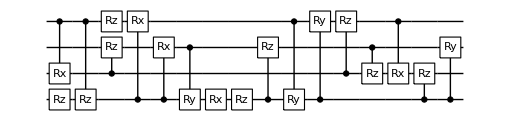

cost=4.2288×10^-8; ngates=18

runtime= 1.17993 minutes

cost=4.2288×10^-8 ;dist=0.000238481; globalphase=5.99906

Cycle1, @Thu 17 Mar 2022 18:02:16, fev:897, <E>: 0.0009614612770590947 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 33, 0, 0, 2}

{{Rz_0[θ_8],C_1[Rx_2[θ_13]],C_2[Rz_1[θ_66]],C_0[Rz_1[θ_58]],C_3[Ry_0[θ_16]],C_0[Rz_2[θ_68]],C_1[Rz_3[θ_60]],Rz_0[θ_83],C_3[Ry_1[θ_63]],C_1[Ry_3[θ_29]],C_0[Rz_3[θ_31]],Ry_3[θ_76],C_2[Ry_3[θ_67]],C_3[Rx_1[θ_57]],C_1[Rx_2[θ_46]],C_3[Rz_1[θ_87]],C_3[Ry_0[θ_49]]},<|θ_8→0.203743,θ_13→-3.14159,θ_16→-3.14159,θ_29→0.32546,θ_31→0.797384,θ_46→3.14159,θ_49→3.14159,θ_57→-3.14159,θ_58→7.09786,θ_60→0.407444,θ_63→3.14159,θ_66→-1.20464,θ_67→-0.0370104,θ_68→10.0735,θ_76→0.0369985,θ_83→-8.5633,θ_87→9.42484|>,{},1975,2,{merged, θsmall, metric, bruteforce}=,{1,68,4,0},Circuit within target precision is found}

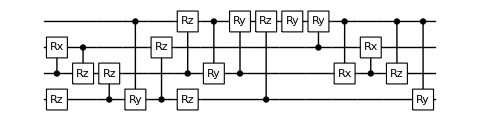

cost=6.78982×10^-9; ngates=17

runtime= 1.84946 minutes

cost=6.78982×10^-9 ;dist=0.000124384; globalphase=4.3256

Cycle1, @Thu 17 Mar 2022 18:03:35, fev:648, <E>: 0.01962750936536073 nansatz:13 merged-smallθ,metric,bf,gmerged: {1, 36, 0, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 18:03:48, fev:741, <E>: 0.01962750936536073 nansatz:13 merged-smallθ,metric,bf,gmerged: {1, 36, 0, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:04:03, fev:835, <E>: 0.01962750936536073 nansatz:13 merged-smallθ,metric,bf,gmerged: {1, 36, 0, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0196275

{{Rz_0[θ_14],C_3[Rz_2[θ_8]],C_1[Rz_2[θ_18]],Rz_1[θ_22],C_1[Rz_0[θ_24]],C_2[Rz_0[θ_32]],Rz_0[θ_35],C_3[Rz_2[θ_38]],C_2[Rz_1[θ_40]],C_3[Rx_2[θ_41]],C_3[Rx_2[θ_46]],C_3[Rz_1[θ_49]],C_2[Rz_1[θ_50]]},<|θ_8→-0.00368055,θ_14→-0.15393,θ_18→-0.898067,θ_22→-1.07566,θ_24→-0.13828,θ_32→1.40982,θ_35→-1.27926,θ_38→0.902296,θ_40→0.58927,θ_41→-1.17668,θ_46→1.17668,θ_49→-1.05688,θ_50→1.02415|>,{2,3},902,3,{merged, θsmall, metric, bruteforce}=,{1,36,0,0},Compilation is either converging or stuck. }

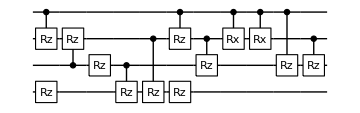

cost=0.0196275; ngates=13

runtime= 0.802441 minutes

cost=0.0196275 ;dist=0.180963; globalphase=0.250083

Cycle1, @Thu 17 Mar 2022 18:04:32, fev:520, <E>: 0.019627500140405818 nansatz:6 merged-smallθ,metric,bf,gmerged: {1, 38, 4, 1, 1}

Cycle2, @Thu 17 Mar 2022 18:04:55, fev:905, <E>: 0.0029196458767853928 nansatz:13 merged-smallθ,metric,bf,gmerged: {1, 66, 9, 1, 1}

{{C_2[Rz_3[θ_107]],C_0[Ry_3[θ_54]],C_0[Rx_2[θ_56]],C_3[Rz_0[θ_116]],C_1[Ry_0[θ_62]],Ry_1[θ_97],C_0[Rz_3[θ_93]],C_2[Rx_1[θ_96]],C_0[Rz_1[θ_123]],Ry_1[θ_92],Rx_1[θ_130],C_1[Ry_0[θ_66]],C_0[Rx_2[θ_82]],C_3[Rz_2[θ_115]],C_0[Rz_1[θ_103]],C_0[Rx_3[θ_114]],C_2[Rz_3[θ_122]]},<|θ_54→-3.14196,θ_56→3.14159,θ_62→3.14159,θ_66→-3.14159,θ_82→-3.14159,θ_92→1.31989,θ_93→1.3896,θ_96→-1.79377,θ_97→-1.33794,θ_103→0.796245,θ_107→-1.37729,θ_114→-3.14117,θ_115→2.0031,θ_116→0.372644,θ_122→2.37831,θ_123→-0.386731,θ_130→0.375993|>,{},1756,3,{merged, θsmall, metric, bruteforce}=,{1,96,11,4},Circuit within target precision is found}

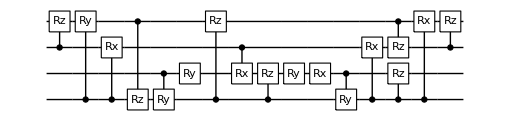

cost=6.59642×10^-8; ngates=17

runtime= 1.50317 minutes

cost=6.59642×10^-8 ;dist=0.000382806; globalphase=6.27407

{{C_2[Rz_0[θ_2]],Rz_3[θ_5],C_0[Ry_3[θ_6]],C_1[Rx_0[θ_7]],C_2[Rx_1[θ_10]],C_3[Ry_2[θ_11]],Ry_2[θ_20],C_0[Ry_3[θ_14]],C_0[Rz_1[θ_18]],C_3[Ry_0[θ_23]],Rz_1[θ_24],C_1[Rz_2[θ_32]],C_1[Ry_3[θ_38]],C_3[Rx_2[θ_39]],C_2[Rx_1[θ_40]],C_2[Ry_3[θ_41]],C_2[Rz_0[θ_42]],C_0[Rz_2[θ_47]],C_3[Ry_0[θ_49]]},<|θ_2→-3.28302,θ_5→-3.11554,θ_6→-3.14159,θ_7→-3.14159,θ_10→-3.14159,θ_11→4.78929,θ_14→3.14159,θ_18→11.0783,θ_20→-4.83362,θ_23→-3.14159,θ_24→5.54095,θ_32→1.57387,θ_38→3.14159,θ_39→-6.32752,θ_40→-3.14159,θ_41→-3.14159,θ_42→-6.27238,θ_47→4.80068,θ_49→3.14159|>,{},1787,1,{merged, θsmall, metric, bruteforce}=,{0,31,0,0},Circuit within target precision is found}

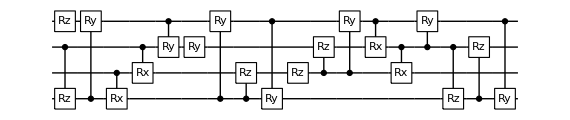

cost=2.12375×10^-9; ngates=19

runtime= 1.44013 minutes

cost=2.12375×10^-9 ;dist=0.000068049; globalphase=4.11687

Cycle1, @Thu 17 Mar 2022 18:09:42, fev:2807, <E>: 0.02858219574800014 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 23, 3, 0, 2}

{{Rz_2[θ_32],C_0[Rx_2[θ_36]],Rz_2[θ_18],C_1[Ry_0[θ_22]],C_3[Ry_1[θ_85]],C_3[Rz_2[θ_53]],C_3[Ry_1[θ_43]],C_1[Rx_0[θ_46]],C_2[Ry_3[θ_8]],C_3[Ry_0[θ_19]],C_1[Rx_3[θ_34]],C_3[Ry_1[θ_10]],C_2[Rz_1[θ_44]],C_0[Rz_2[θ_68]],C_2[Rz_0[θ_42]],Ry_0[θ_56],C_1[Ry_0[θ_6]],C_3[Rx_0[θ_7]],Rz_0[θ_74],Rx_0[θ_16],C_0[Rz_1[θ_63]],C_0[Ry_2[θ_65]],C_0[Rz_2[θ_38]]},<|θ_6→-1.57132,θ_7→3.14124,θ_8→-0.702792,θ_10→-3.14159,θ_16→0.785656,θ_18→-2.45371,θ_19→3.14021,θ_22→-3.14135,θ_32→0.0415046,θ_34→0.746899,θ_36→-3.14159,θ_38→0.110399,θ_42→-1.62099,θ_43→1.22507,θ_44→4.56836,θ_46→4.71241,θ_53→0.0841908,θ_56→-0.785275,θ_63→-2.9635,θ_65→-3.14159,θ_68→6.38431,θ_74→-1.57017,θ_85→1.91652|>,{},4825,2,{merged, θsmall, metric, bruteforce}=,{1,63,3,0},Circuit within target precision is found}

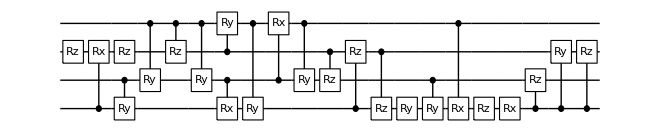

cost=7.7002×10^-8; ngates=23

runtime= 4.71089 minutes

cost=7.7002×10^-8 ;dist=0.000344645; globalphase=5.64287

Cycle1, @Thu 17 Mar 2022 18:13:16, fev:1397, <E>: 1.6274041069186396e-6 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 27, 0, 0, 4}

{{C_2[Ry_1[θ_7]],C_2[Ry_0[θ_9]],C_3[Rz_2[θ_11]],C_1[Rz_3[θ_21]],Rx_1[θ_29],C_2[Ry_3[θ_26]],C_0[Ry_2[θ_28]],Rx_3[θ_53],C_1[Ry_2[θ_30]],C_0[Rx_1[θ_35]],Ry_1[θ_37],C_0[Ry_1[θ_40]],C_1[Rz_0[θ_42]],C_2[Rx_1[θ_45]],C_2[Ry_0[θ_47]],C_0[Rz_2[θ_52]],C_2[Rx_3[θ_60]],C_1[Rz_0[θ_70]],C_2[Ry_3[θ_61]],Rx_3[θ_64],C_0[Rz_3[θ_87]]},<|θ_7→3.14159,θ_9→3.14159,θ_11→-3.14153,θ_21→-6.19373,θ_26→-3.14161,θ_28→0.0443246,θ_29→3.14159,θ_30→-1.49401,θ_35→-3.14159,θ_37→-3.14159,θ_40→3.14159,θ_42→3.1853,θ_45→3.14159,θ_47→-3.14159,θ_52→0.193392,θ_53→-1.57082,θ_60→-3.14163,θ_61→1.64635,θ_64→1.57082,θ_70→-3.05224,θ_87→-1.54222|>,{},2452,2,{merged, θsmall, metric, bruteforce}=,{0,63,5,1},Circuit within target precision is found}

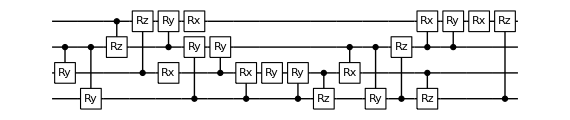

cost=1.21313×10^-8; ngates=21

runtime= 2.24894 minutes

cost=1.21313×10^-8 ;dist=0.000165695; globalphase=2.10128

{{C_1[Ry_3[θ_2]],C_2[Ry_0[θ_4]],C_0[Rx_2[θ_5]],C_1[Rz_2[θ_7]],C_3[Ry_2[θ_12]],C_3[Ry_1[θ_13]],Rz_2[θ_15],C_2[Rz_1[θ_17]],C_3[Ry_2[θ_20]],C_0[Rx_2[θ_22]],C_0[Rz_2[θ_23]],C_1[Rx_2[θ_26]],C_1[Ry_2[θ_28]],C_0[Rx_1[θ_29]],C_2[Rz_0[θ_31]],C_1[Ry_2[θ_33]],C_1[Ry_3[θ_36]],C_0[Rx_2[θ_35]],C_0[Rz_1[θ_37]],C_1[Rz_0[θ_38]],C_1[Rx_2[θ_39]],C_0[Rx_2[θ_45]],C_2[Rz_0[θ_46]],C_2[Ry_0[θ_47]]},<|θ_2→3.14159,θ_4→-3.14159,θ_5→-1.57074,θ_7→3.14183,θ_12→4.73169,θ_13→-1.57576,θ_15→-0.38979,θ_17→7.93094,θ_20→3.08789,θ_22→3.28523,θ_23→5.84608,θ_26→1.49426,θ_28→1.57242,θ_29→-1.57144,θ_31→-2.98929,θ_33→-4.71246,θ_35→0.60512,θ_36→3.14159,θ_37→-3.01686,θ_38→2.69355,θ_39→3.14125,θ_45→4.10752,θ_46→-4.52366,θ_47→-3.14159|>,{},1964,1,{merged, θsmall, metric, bruteforce}=,{0,26,0,0},Circuit within target precision is found}

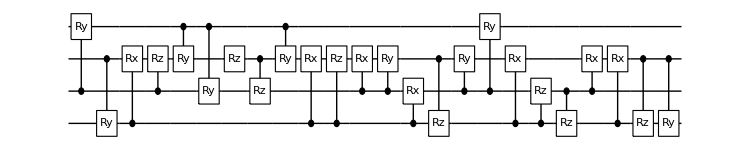

cost=2.57724×10^-9; ngates=24

runtime= 2.00549 minutes

cost=2.57724×10^-9 ;dist=0.0000767625; globalphase=4.86081

Cycle1, @Thu 17 Mar 2022 18:17:00, fev:724, <E>: 0.16072503669972393 nansatz:31 merged-smallθ,metric,bf,gmerged: {0, 19, 0, 0, 2}

Cycle2, @Thu 17 Mar 2022 18:17:43, fev:1235, <E>: 0.00008431233513139791 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 55, 22, 0, 5}

{{C_0[Rx_1[θ_105]],C_3[Rz_2[θ_16]],C_0[Rx_1[θ_108]],C_2[Ry_3[θ_51]],C_3[Rz_0[θ_57]],C_2[Rx_1[θ_60]],C_0[Ry_2[θ_68]],C_3[Rz_1[θ_101]],C_2[Rz_0[θ_112]],Ry_0[θ_76],C_2[Rz_3[θ_75]],Rx_0[θ_98],C_3[Rz_0[θ_124]],C_1[Rx_0[θ_111]],C_1[Ry_0[θ_79]],C_0[Ry_2[θ_80]],C_3[Ry_0[θ_121]],C_2[Rx_1[θ_82]],C_3[Ry_0[θ_114]],C_0[Rz_3[θ_102]],C_2[Ry_3[θ_84]]},<|θ_16→-2.6608,θ_51→3.14159,θ_57→-7.75299,θ_60→3.14159,θ_68→-3.14159,θ_75→-1.99145,θ_76→-1.2161,θ_79→1.88405,θ_80→3.14159,θ_82→-3.14159,θ_84→-3.14159,θ_98→1.21454,θ_101→-1.72086,θ_102→-0.579283,θ_105→-0.483514,θ_108→0.483514,θ_111→1.97596,θ_112→7.65753,θ_114→-0.485897,θ_121→0.485897,θ_124→-0.0446048|>,{},2451,3,{merged, θsmall, metric, bruteforce}=,{0,87,22,0},Circuit within target precision is found}

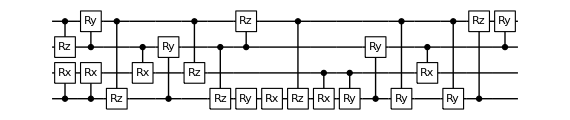

cost=8.79597×10^-8; ngates=21

runtime= 2.56099 minutes

cost=8.79597×10^-8 ;dist=0.00046372; globalphase=1.78331

Cycle1, @Thu 17 Mar 2022 18:19:53, fev:945, <E>: 0.0001638805679012867 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 26, 0, 0, 1}

{{C_1[Rz_0[θ_47]],C_2[Ry_3[θ_19]],C_1[Ry_0[θ_16]],Ry_1[θ_12],C_1[Rz_2[θ_15]],C_2[Rz_3[θ_32]],Ry_1[θ_79],C_3[Rx_2[θ_82]],C_2[Ry_1[θ_48]],Rx_2[θ_85],Rx_1[θ_26],C_3[Ry_2[θ_27]],C_0[Rz_2[θ_29]],C_2[Rx_1[θ_40]],C_3[Rz_0[θ_69]],C_1[Ry_0[θ_2]],C_2[Ry_3[θ_1]],C_2[Rz_0[θ_67]],C_1[Rz_2[θ_28]],C_0[Rz_2[θ_58]]},<|θ_1→3.14159,θ_2→3.14159,θ_12→-1.5708,θ_15→3.14144,θ_16→-3.14159,θ_19→-3.14159,θ_26→1.57082,θ_27→-0.725049,θ_28→-2.91145,θ_29→-4.79944,θ_32→1.34761,θ_40→-3.14159,θ_47→1.48106,θ_48→-9.52502,θ_58→1.73816,θ_67→1.79452,θ_69→1.25471,θ_79→-7.03841,θ_82→0.725882,θ_85→-0.044373|>,{},2291,2,{merged, θsmall, metric, bruteforce}=,{0,62,6,1},Circuit within target precision is found}

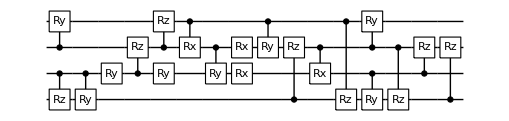

cost=4.76339×10^-8; ngates=20

runtime= 2.28685 minutes

cost=4.76339×10^-8 ;dist=0.00031872; globalphase=0.783703

Cycle1, @Thu 17 Mar 2022 18:22:24, fev:1500, <E>: 0.006537035700527771 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 0, 0}

{{Rz_2[θ_88],C_1[Ry_0[θ_13]],C_3[Ry_1[θ_22]],C_1[Rz_2[θ_76]],C_1[Rx_0[θ_26]],C_2[Rz_3[θ_78]],C_0[Rx_1[θ_27]],C_3[Rz_1[θ_81]],C_3[Rx_2[θ_64]],C_1[Ry_3[θ_33]],C_3[Rz_0[θ_38]],C_0[Ry_3[θ_73]],C_2[Rz_0[θ_82]],C_1[Rx_3[θ_40]],C_2[Rz_3[θ_42]],C_3[Rx_0[θ_44]],C_3[Ry_2[θ_45]],C_3[Rz_1[θ_46]],C_0[Rx_1[θ_49]]},<|θ_13→3.14159,θ_22→-3.14159,θ_26→-3.14159,θ_27→-3.14159,θ_33→0.725677,θ_38→3.04155,θ_40→0.72454,θ_42→-7.80598,θ_44→3.14159,θ_45→-3.14159,θ_46→2.97864,θ_49→-3.14159,θ_64→3.14159,θ_73→-0.0443217,θ_76→3.2752,θ_78→-4.58365,θ_81→-2.23397,θ_82→-0.67476,θ_88→-6.65084|>,{},2364,2,{merged, θsmall, metric, bruteforce}=,{0,67,4,0},Circuit within target precision is found}

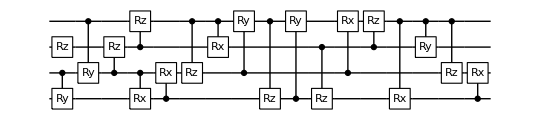

cost=4.62961×10^-8; ngates=19

runtime= 1.9723 minutes

cost=4.62961×10^-8 ;dist=0.000346108; globalphase=1.52199

Cycle1, @Thu 17 Mar 2022 18:23:32, fev:454, <E>: 0.16072501687286556 nansatz:17 merged-smallθ,metric,bf,gmerged: {1, 32, 0, 0, 3}

Cycle2, @Thu 17 Mar 2022 18:24:22, fev:1319, <E>: 0.05544745926547079 nansatz:15 merged-smallθ,metric,bf,gmerged: {1, 72, 2, 0, 5}

{{C_0[Rz_3[θ_80]],C_1[Rz_0[θ_114]],C_2[Rx_1[θ_62]],C_3[Ry_0[θ_82]],Rx_1[θ_97],C_3[Rx_2[θ_90]],C_2[Rx_3[θ_106]],C_3[Rz_0[θ_128]],C_1[Rz_0[θ_100]],C_2[Rx_3[θ_59]],C_3[Rx_1[θ_89]],Rx_3[θ_102],C_3[Rz_2[θ_115]],C_2[Rx_3[θ_75]],C_0[Rx_3[θ_126]],C_3[Rx_2[θ_83]],C_0[Ry_1[θ_104]],C_3[Rz_2[θ_29]],C_2[Rz_1[θ_30]],C_3[Rx_0[θ_38]],Ry_1[θ_91]},<|θ_29→-0.592668,θ_30→-3.1415,θ_38→-3.14159,θ_59→2.15438,θ_62→-9.42478,θ_75→-5.00875,θ_80→-3.14402,θ_82→-3.14159,θ_83→3.14159,θ_89→4.79498,θ_90→-3.14159,θ_91→-1.57075,θ_97→1.57084,θ_100→-3.14133,θ_102→-2.48823,θ_104→3.14156,θ_106→-1.14258,θ_114→-4.19576,θ_115→-0.134445,θ_126→2.50643,θ_128→1.68933|>,{},3223,3,{merged, θsmall, metric, bruteforce}=,{1,101,6,0},Circuit within target precision is found}

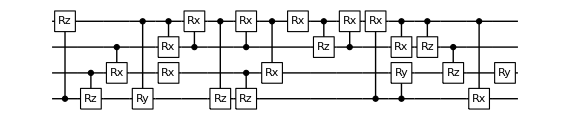

cost=4.82515×10^-8; ngates=21

runtime= 3.34569 minutes

cost=4.82515×10^-8 ;dist=0.000278827; globalphase=2.51077

Cycle1, @Thu 17 Mar 2022 18:27:00, fev:568, <E>: 0.16072504035210478 nansatz:9 merged-smallθ,metric,bf,gmerged: {2, 38, 0, 1, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 18:27:13, fev:672, <E>: 0.16072504035210478 nansatz:9 merged-smallθ,metric,bf,gmerged: {2, 38, 0, 1, 2}

Cycle3, @Thu 17 Mar 2022 18:28:17, fev:1646, <E>: 0.000920912580990807 nansatz:17 merged-smallθ,metric,bf,gmerged: {2, 72, 5, 1, 5}

{{C_2[Ry_0[θ_88]],C_3[Rz_1[θ_72]],C_1[Ry_3[θ_91]],C_0[Ry_2[θ_89]],Rx_3[θ_76],C_2[Ry_1[θ_73]],C_3[Rz_2[θ_112]],C_1[Ry_2[θ_68]],C_0[Rz_2[θ_20]],C_0[Rx_2[θ_120]],C_1[Ry_2[θ_64]],C_2[Ry_1[θ_90]],C_3[Ry_2[θ_56]],C_2[Rz_1[θ_113]],Ry_2[θ_59],C_1[Ry_3[θ_129]],C_1[Rx_3[θ_118]],Ry_3[θ_48],C_2[Rz_1[θ_123]],C_0[Rz_2[θ_109]],C_1[Rx_3[θ_92]],C_2[Ry_0[θ_63]],Ry_3[θ_111]},<|θ_20→8.44933,θ_48→-2.78489,θ_56→-3.14159,θ_59→3.14159,θ_63→3.14159,θ_64→-5.4228,θ_68→5.42285,θ_72→1.72966,θ_73→-3.14159,θ_76→3.14159,θ_88→-3.14159,θ_89→-3.14159,θ_90→3.14159,θ_91→-3.14159,θ_92→3.65371,θ_109→-1.06721,θ_111→-0.356686,θ_112→-0.502704,θ_113→0.401813,θ_118→0.619551,θ_120→-0.0444032,θ_123→0.222073,θ_129→-0.659182|>,{2},3116,4,{merged, θsmall, metric, bruteforce}=,{2,109,10,1},Circuit within target precision is found}

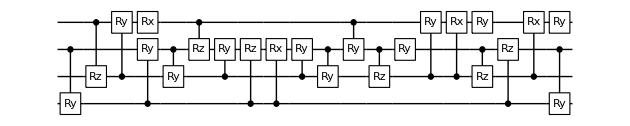

cost=7.80786×10^-8; ngates=23

runtime= 3.18361 minutes

cost=7.80786×10^-8 ;dist=0.000357743; globalphase=0.189912

Cycle1, @Thu 17 Mar 2022 18:30:07, fev:491, <E>: 0.16065070579517948 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 2}

Cycle2, @Thu 17 Mar 2022 18:30:52, fev:1155, <E>: 0.001645970321343837 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 72, 4, 0, 2}

{{C_1[Rz_0[θ_125]],C_2[Rz_1[θ_40]],C_2[Rz_3[θ_97]],C_1[Rx_2[θ_36]],C_3[Rz_0[θ_95]],C_0[Ry_3[θ_22]],C_0[Rx_1[θ_64]],C_2[Rx_0[θ_111]],C_1[Rx_0[θ_44]],C_2[Rx_1[θ_87]],C_1[Rz_0[θ_73]],C_2[Rx_1[θ_7]],C_1[Rx_0[θ_34]],C_0[Rz_3[θ_93]],C_0[Ry_3[θ_38]],C_0[Rx_1[θ_66]],C_3[Rz_0[θ_124]],C_1[Rx_2[θ_23]]},<|θ_7→-3.14159,θ_22→-3.14159,θ_23→-3.14159,θ_34→4.88278,θ_36→3.14159,θ_38→3.14159,θ_40→-5.00818,θ_44→-4.83852,θ_64→3.14159,θ_66→-3.14159,θ_73→-1.46839,θ_87→3.14159,θ_93→-0.316675,θ_95→3.10119,θ_97→-0.0519737,θ_111→-0.0442699,θ_124→3.03998,θ_125→1.6816|>,{},2167,3,{merged, θsmall, metric, bruteforce}=,{0,101,10,0},Circuit within target precision is found}

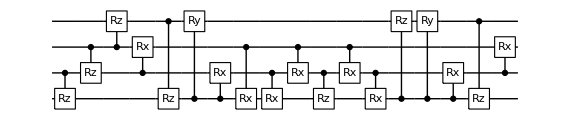

cost=4.75547×10^-8; ngates=18

runtime= 1.76546 minutes

cost=4.75547×10^-8 ;dist=0.000299424; globalphase=4.49485

```mathematica
Table[
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{10}];
,{t,times}];
```

### Full space compilation: {0.001,0.01,0.1,1,4}

```mathematica
resfullH2=<||>;
DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→50,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→0.001,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

{{C_2[Rz_0[θ_13]],Rz_1[θ_25],C_2[Rx_0[θ_30]],C_0[Rz_1[θ_24]],C_1[Rz_0[θ_23]],C_1[Ry_3[θ_47]],C_2[Rz_0[θ_3]],C_1[Ry_3[θ_1]],C_2[Ry_0[θ_20]],C_3[Rz_1[θ_5]],C_0[Rz_3[θ_2]],C_2[Rz_0[θ_11]],C_3[Rz_1[θ_35]],C_2[Rx_0[θ_22]],C_3[Rz_2[θ_18]],C_1[Rz_0[θ_28]],C_1[Rz_0[θ_40]]},<|θ_1→-0.00777598,θ_2→0.000778725,θ_3→0.471014,θ_5→0.842991,θ_11→-0.991329,θ_13→0.520901,θ_18→0.000795691,θ_20→-0.00372539,θ_22→0.00680432,θ_23→0.117774,θ_24→0.00182092,θ_25→-0.00149465,θ_28→-0.111101,θ_30→-0.0043208,θ_35→-0.842508,θ_40→-0.00783091,θ_47→0.00777599|>,{},235,1,{merged, θsmall, metric, bruteforce}=,{0,27,6,0},Circuit within target precision is found}

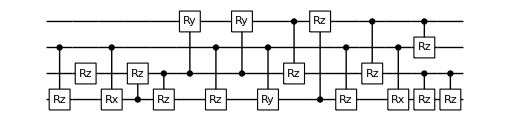

cost=5.38599×10^-8; ngates=17

runtime= 0.186038 minutes

cost=5.38599×10^-8 ;dist=0.000439642; globalphase=6.28319

{{C_0[Rz_1[θ_6]],C_2[Rz_0[θ_8]],C_2[Rz_1[θ_9]],C_0[Rz_3[θ_12]],Rz_1[θ_14],C_0[Rz_2[θ_23]],C_0[Ry_3[θ_32]],C_0[Ry_3[θ_37]]},<|θ_6→0.000605047,θ_8→-0.000664284,θ_9→0.00130057,θ_12→0.000681692,θ_14→-0.00132091,θ_23→0.00112871,θ_32→-0.000670315,θ_37→0.000671277|>,{},232,1,{merged, θsmall, metric, bruteforce}=,{0,35,7,0},Circuit within target precision is found}

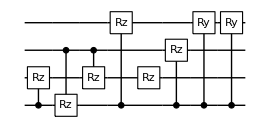

cost=8.53224×10^-8; ngates=8

runtime= 0.161901 minutes

cost=8.53224×10^-8 ;dist=0.000548408; globalphase=0.00023339

{{C_1[Rz_0[θ_20]],C_0[Rz_1[θ_4]],C_0[Rz_3[θ_24]],C_1[Rz_2[θ_31]],C_3[Rz_0[θ_43]],Rz_3[θ_12]},<|θ_4→-0.000681613,θ_12→-0.00088162,θ_20→0.00131735,θ_24→0.00263301,θ_31→0.000942395,θ_43→-0.00197917|>,{},177,1,{merged, θsmall, metric, bruteforce}=,{0,31,13,0},Circuit within target precision is found}

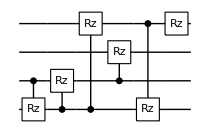

cost=7.29057×10^-8; ngates=6

runtime= 0.118483 minutes

cost=7.29057×10^-8 ;dist=0.000522835; globalphase=0.000248541

{{Rz_3[θ_9],C_3[Rz_1[θ_21]],Rz_1[θ_35],C_2[Rz_3[θ_30]],C_1[Rz_2[θ_36]],C_1[Rz_3[θ_37]],C_0[Rz_3[θ_44]],C_3[Rz_0[θ_49]]},<|θ_9→0.0326502,θ_21→0.0669361,θ_30→0.000697656,θ_35→-0.033811,θ_36→0.000579523,θ_37→-0.0664536,θ_44→0.00134937,θ_49→-0.000685657|>,{},165,1,{merged, θsmall, metric, bruteforce}=,{0,37,5,0},Circuit within target precision is found}

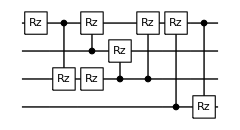

cost=5.78289×10^-8; ngates=8

runtime= 0.114116 minutes

cost=5.78289×10^-8 ;dist=0.000427377; globalphase=0.000135482

{{C_0[Ry_2[θ_31]],C_0[Rz_3[θ_23]],C_0[Rz_3[θ_18]],C_1[Ry_3[θ_28]],C_1[Ry_2[θ_29]],C_0[Ry_3[θ_3]],Rz_0[θ_19],C_1[Ry_3[θ_34]],C_3[Rz_2[θ_26]],C_1[Rz_0[θ_8]],C_1[Ry_3[θ_1]],C_0[Rz_1[θ_9]],C_0[Ry_3[θ_15]],C_1[Ry_2[θ_50]],C_0[Ry_2[θ_40]],C_1[Rz_0[θ_7]]},<|θ_1→-0.0171327,θ_3→0.222593,θ_7→-0.00105486,θ_8→0.00289219,θ_9→-0.00104703,θ_15→-0.222733,θ_18→-0.00150527,θ_19→-0.00114621,θ_23→0.0023986,θ_26→0.000791027,θ_28→-0.0123251,θ_29→0.0016111,θ_31→-0.00047941,θ_34→0.0294951,θ_40→0.000479387,θ_50→-0.00130632|>,{},193,1,{merged, θsmall, metric, bruteforce}=,{0,22,12,0},Circuit within target precision is found}

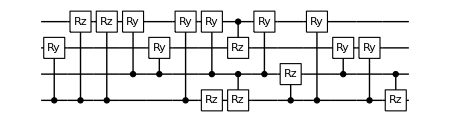

cost=9.61803×10^-8; ngates=16

runtime= 0.17817 minutes

cost=9.61803×10^-8 ;dist=0.000558463; globalphase=0.000139709

{{Rx_2[θ_1],C_1[Rz_3[θ_2]],Rx_3[θ_5],Rz_2[θ_12],C_1[Ry_3[θ_7]],Rx_2[θ_29],C_3[Rz_1[θ_15]],C_0[Rz_3[θ_16]],C_1[Ry_3[θ_19]],Ry_3[θ_22],Rx_3[θ_23],C_1[Ry_3[θ_27]],C_1[Rz_2[θ_30]],Ry_3[θ_38],Ry_2[θ_33],C_1[Rx_3[θ_45]],C_3[Rz_2[θ_46]],Ry_2[θ_48],C_0[Rz_2[θ_50]]},<|θ_1→-0.865415,θ_2→-0.00341436,θ_5→0.00452011,θ_7→1.07413,θ_12→-0.000732491,θ_15→-0.000500807,θ_16→0.000283639,θ_19→-2.34,θ_22→-0.00234886,θ_23→-0.0045137,θ_27→1.26595,θ_29→0.865423,θ_30→0.000663708,θ_33→0.0218416,θ_38→0.00236072,θ_45→-0.00307872,θ_46→0.000697473,θ_48→-0.0223993,θ_50→0.000482498|>,{},236,1,{merged, θsmall, metric, bruteforce}=,{0,28,3,0},Circuit within target precision is found}

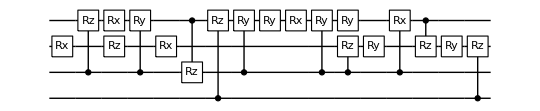

cost=9.73917×10^-8; ngates=19

runtime= 0.169643 minutes

cost=9.73917×10^-8 ;dist=0.000488272; globalphase=6.28319

{{C_1[Rz_3[θ_6]],Rz_3[θ_45],Rz_1[θ_5],C_2[Rx_3[θ_30]],C_3[Rz_2[θ_11]],C_2[Rx_3[θ_39]],C_1[Rz_2[θ_21]],Rz_3[θ_49],C_2[Rz_1[θ_37]],C_0[Rz_1[θ_16]]},<|θ_5→-0.00113467,θ_6→0.000480226,θ_11→0.0010751,θ_16→0.000679015,θ_21→-0.000216736,θ_30→0.379584,θ_37→0.000900588,θ_39→-0.379577,θ_45→0.384071,θ_49→-0.383668|>,{},326,1,{merged, θsmall, metric, bruteforce}=,{1,30,6,2},Circuit within target precision is found}

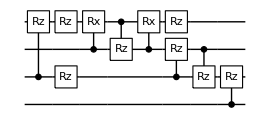

cost=9.97887×10^-8; ngates=10

runtime= 0.218724 minutes

cost=9.97887×10^-8 ;dist=0.000518139; globalphase=0.00015234

{{Rz_1[θ_8],C_0[Rx_3[θ_34]],C_1[Rz_2[θ_23]],C_3[Rz_1[θ_46]],Rx_3[θ_49],C_3[Rz_0[θ_41]],Rx_3[θ_16],C_0[Rx_3[θ_7]],C_1[Rz_3[θ_28]],C_2[Rz_3[θ_42]],C_0[Rz_3[θ_39]]},<|θ_7→0.00596456,θ_8→-0.00106899,θ_16→0.353835,θ_23→0.00076806,θ_28→-0.00100807,θ_34→-0.00596408,θ_39→0.00123731,θ_41→-0.000611333,θ_42→0.00118231,θ_46→0.00149365,θ_49→-0.353828|>,{},291,1,{merged, θsmall, metric, bruteforce}=,{0,33,5,1},Circuit within target precision is found}

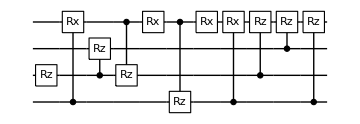

cost=8.76822×10^-8; ngates=11

runtime= 0.196129 minutes

cost=8.76822×10^-8 ;dist=0.000529562; globalphase=0.000103902

{{C_3[Rz_1[θ_44]],C_2[Ry_0[θ_5]],C_1[Rz_3[θ_9]],C_2[Ry_0[θ_45]],Rz_1[θ_37],C_1[Ry_3[θ_8]],C_1[Ry_3[θ_31]],C_1[Ry_3[θ_39]],C_1[Rz_3[θ_1]],C_1[Rz_3[θ_3]],C_0[Rz_1[θ_38]],C_1[Rz_3[θ_18]],C_1[Rz_3[θ_27]],Rz_1[θ_35],C_0[Rz_1[θ_50]],C_0[Rz_3[θ_32]],C_3[Rz_2[θ_2]],C_3[Rz_1[θ_34]]},<|θ_1→0.414871,θ_2→0.000795621,θ_3→0.14669,θ_5→0.23438,θ_8→0.143378,θ_9→-0.81632,θ_18→0.432359,θ_27→-0.17779,θ_31→0.878746,θ_32→0.000858878,θ_34→-0.0800261,θ_35→0.946487,θ_37→-0.94754,θ_38→0.0717111,θ_39→-1.02212,θ_44→0.0807706,θ_45→-0.23438,θ_50→-0.0710363|>,{},286,1,{merged, θsmall, metric, bruteforce}=,{1,29,0,2},Circuit within target precision is found}

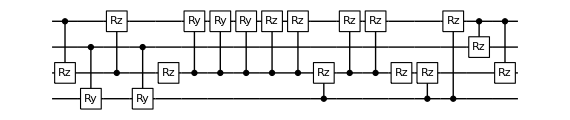

cost=8.67593×10^-8; ngates=18

runtime= 0.219888 minutes

cost=8.67593×10^-8 ;dist=0.000568077; globalphase=0.0000842063

{{C_3[Rz_1[θ_5]],Rz_0[θ_9],C_2[Rx_3[θ_8]],Rz_2[θ_15],C_3[Rz_0[θ_16]],C_0[Rz_1[θ_17]],C_1[Rz_2[θ_23]],C_2[Rz_1[θ_30]],C_2[Rx_3[θ_35]],Rz_1[θ_37],C_2[Rx_3[θ_45]],C_1[Rz_3[θ_48]]},<|θ_5→-0.000807964,θ_8→0.378061,θ_9→-0.000662963,θ_15→-0.209555,θ_16→0.000640275,θ_17→0.000681059,θ_23→0.420004,θ_30→-0.419336,θ_35→-0.369465,θ_37→0.209386,θ_45→-0.00859527,θ_48→0.00132482|>,{},256,1,{merged, θsmall, metric, bruteforce}=,{2,35,0,1},Circuit within target precision is found}

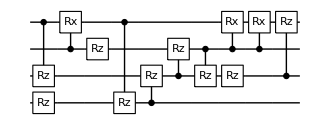

cost=6.67842×10^-8; ngates=12

runtime= 0.153003 minutes

cost=6.67842×10^-8 ;dist=0.00045604; globalphase=0.000131999

Cycle1, @Thu 17 Mar 2022 18:34:08, fev:473, <E>: 8.287686844576925e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {1, 30, 0, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 18:34:23, fev:581, <E>: 8.287686844576925e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {1, 30, 0, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:34:40, fev:675, <E>: 8.287686844576925e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {1, 30, 0, 0, 8}

I'm slowing down. Number of gates is increased to 70 @cycle 4

Cycle4, @Thu 17 Mar 2022 18:35:08, fev:788, <E>: 8.287686844576925e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {1, 30, 0, 0, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=8.28769×10^-7

{{C_2[Rz_3[θ_25]],C_0[Rz_3[θ_30]],C_2[Rz_0[θ_41]],C_3[Rz_1[θ_4]],C_3[Rz_0[θ_13]],C_0[Rz_2[θ_22]],C_2[Rz_1[θ_12]],C_1[Rz_2[θ_21]],Rz_1[θ_32],Rz_2[θ_49],C_1[Ry_0[θ_40]],C_1[Ry_0[θ_50]],C_2[Rz_1[θ_10]],C_1[Rx_3[θ_46]],C_1[Rz_2[θ_35]],C_1[Rz_0[θ_27]],C_1[Rx_3[θ_6]]},<|θ_4→0.00480454,θ_6→0.0465172,θ_10→1.90611,θ_12→-0.330184,θ_13→0.00505896,θ_21→-0.446585,θ_22→0.0239356,θ_25→0.00709438,θ_27→0.00695021,θ_30→0.00171772,θ_32→-0.793817,θ_35→-1.12271,θ_40→0.138772,θ_41→-0.0190268,θ_46→-0.0465172,θ_49→0.777145,θ_50→-0.138772|>,{2,3,4},850,4,{merged, θsmall, metric, bruteforce}=,{1,30,0,0},Compilation is either converging or stuck. }

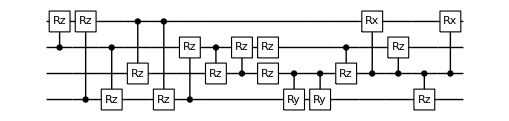

cost=8.28769×10^-7; ngates=17

runtime= 1.46108 minutes

cost=8.28769×10^-7 ;dist=0.00185917; globalphase=0.000954393

Cycle1, @Thu 17 Mar 2022 18:35:48, fev:613, <E>: 1.006304241601974e-6 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 32, 0, 0, 3}

Cycle2, @Thu 17 Mar 2022 18:36:37, fev:1406, <E>: 8.423311048666449e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 52, 6, 0, 6}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:37:00, fev:1515, <E>: 8.423311048666449e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 52, 6, 0, 7}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Thu 17 Mar 2022 18:37:28, fev:1623, <E>: 8.423311048666449e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 52, 6, 0, 9}

I'm slowing down. Number of gates is increased to 70 @cycle 5

Cycle5, @Thu 17 Mar 2022 18:38:05, fev:1736, <E>: 8.423311048666449e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 52, 6, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=8.42331×10^-7

{{C_0[Rz_1[θ_6]],Rx_3[θ_1],C_2[Rz_0[θ_9]],C_3[Rz_0[θ_18]],C_0[Ry_3[θ_10]],C_3[Rz_1[θ_13]],Rx_3[θ_34],C_3[Rz_2[θ_46]],C_1[Rz_2[θ_5]],C_0[Rz_3[θ_15]],C_2[Rz_1[θ_33]],C_0[Ry_3[θ_54]],C_2[Rx_1[θ_52]],C_2[Rx_3[θ_57]],C_2[Ry_1[θ_60]],Rz_2[θ_61],C_3[Rz_1[θ_63]],C_2[Rx_3[θ_64]],C_0[Rx_1[θ_65]],C_2[Ry_1[θ_69]],C_0[Rz_3[θ_72]],C_0[Rx_1[θ_73]],C_0[Ry_3[θ_77]],C_2[Rx_1[θ_81]],Rx_3[θ_78],C_1[Rz_0[θ_84]],C_2[Ry_3[θ_85]],C_0[Ry_3[θ_87]],Ry_3[θ_88],C_0[Rz_3[θ_90]]},<|θ_1→-1.77326,θ_5→0.0452309,θ_6→0.0283091,θ_9→0.00480089,θ_10→0.75814,θ_13→-0.00113809,θ_15→-0.869743,θ_18→0.0100474,θ_33→-0.038722,θ_34→1.59497,θ_46→0.00708319,θ_52→-0.13067,θ_54→0.227678,θ_57→0.0013533,θ_60→0.0021936,θ_61→-0.0216874,θ_63→0.00471616,θ_64→-0.0012828,θ_65→0.103995,θ_69→-0.00188607,θ_72→-0.0502289,θ_73→-0.103994,θ_77→-0.441341,θ_78→0.178259,θ_81→0.130674,θ_84→-0.0216807,θ_85→0.00128508,θ_87→0.207132,θ_88→-0.00556275,θ_90→0.207428|>,{3,4,5},1877,5,{merged, θsmall, metric, bruteforce}=,{0,52,6,0},I keep failing to lower the energy. }

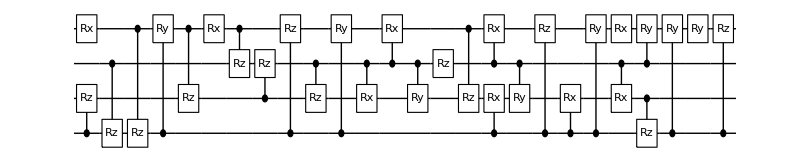

cost=8.42331×10^-7; ngates=30

runtime= 2.91331 minutes

cost=8.42331×10^-7 ;dist=0.00186298; globalphase=0.000992043

Cycle1, @Thu 17 Mar 2022 18:38:34, fev:366, <E>: 8.397415914851436e-7 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 27, 7, 2, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 18:38:47, fev:460, <E>: 8.397415914851436e-7 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 27, 7, 2, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:39:02, fev:552, <E>: 8.397415914851436e-7 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 27, 7, 2, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=8.39742×10^-7

{{C_1[Rz_2[θ_5]],C_0[Rz_1[θ_6]],C_2[Ry_3[θ_7]],C_3[Rx_0[θ_11]],C_2[Rz_1[θ_13]],C_1[Rz_3[θ_14]],C_0[Rz_2[θ_18]],C_3[Rz_1[θ_16]],C_0[Rz_3[θ_19]],C_2[Rz_3[θ_25]],Rz_0[θ_28],C_3[Rx_0[θ_36]],C_2[Ry_3[θ_38]],Rz_2[θ_48]},<|θ_5→0.0297407,θ_6→0.00674627,θ_7→0.0136764,θ_11→-0.132168,θ_13→-0.0231044,θ_14→-0.00467997,θ_16→0.00950291,θ_18→0.00481289,θ_19→0.00664515,θ_25→0.00697324,θ_28→-0.00342282,θ_36→0.132336,θ_38→-0.0136778,θ_48→-0.0128081|>,{2,3},593,3,{merged, θsmall, metric, bruteforce}=,{0,27,7,2},Compilation is either converging or stuck. }

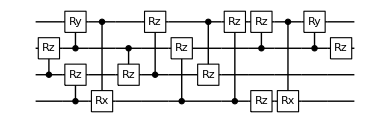

cost=8.39031×10^-7; ngates=14

runtime= 0.829632 minutes

cost=8.39031×10^-7 ;dist=0.00182459; globalphase=0.000980315

Cycle1, @Thu 17 Mar 2022 18:39:33, fev:320, <E>: 8.36734346365553e-7 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 26, 13, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 18:39:41, fev:399, <E>: 8.36734346365553e-7 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 26, 13, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:39:55, fev:496, <E>: 8.36734346365553e-7 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 26, 13, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=8.36734×10^-7

{{C_2[Rz_3[θ_2]],C_2[Rz_0[θ_29]],C_3[Rz_0[θ_5]],C_2[Rz_1[θ_11]],C_1[Rz_3[θ_46]],Rz_0[θ_25],C_0[Rz_1[θ_12]],C_1[Rz_2[θ_10]],C_0[Rz_2[θ_13]],C_3[Rz_2[θ_9]]},<|θ_2→0.00376096,θ_5→0.00664113,θ_9→0.00337,θ_10→0.020747,θ_11→-0.0139553,θ_12→0.0069275,θ_13→-0.0149199,θ_25→-0.0166312,θ_29→0.0198388,θ_46→0.00500494|>,{2,3},520,3,{merged, θsmall, metric, bruteforce}=,{0,26,13,0},Compilation is either converging or stuck. }

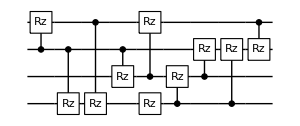

cost=8.36734×10^-7; ngates=10

runtime= 0.758245 minutes

cost=8.36734×10^-7 ;dist=0.00185665; globalphase=0.000902207

Cycle1, @Thu 17 Mar 2022 18:40:33, fev:535, <E>: 1.335993983664352e-6 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 24, 8, 0, 1}

Cycle2, @Thu 17 Mar 2022 18:41:07, fev:962, <E>: 8.31126739320176e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 57, 8, 0, 5}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:41:22, fev:1057, <E>: 8.31126739320176e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 57, 8, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Thu 17 Mar 2022 18:41:39, fev:1154, <E>: 8.31126739320176e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 57, 8, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=8.31127×10^-7

{{C_1[Rz_2[θ_26]],Rz_2[θ_12],C_1[Rx_3[θ_6]],Rz_3[θ_19],C_0[Rz_2[θ_13]],C_1[Rx_3[θ_37]],C_0[Rz_3[θ_32]],Rz_3[θ_51],Rz_0[θ_58],C_1[Ry_3[θ_52]],C_2[Rz_3[θ_53]],C_3[Rz_2[θ_55]],C_1[Ry_2[θ_61]],C_0[Rz_3[θ_62]],C_1[Ry_2[θ_68]],C_1[Rz_2[θ_69]],C_1[Rz_0[θ_71]],C_2[Rz_0[θ_74]],C_0[Rx_3[θ_75]],Rz_2[θ_80],C_1[Rx_3[θ_83]],C_0[Rx_3[θ_84]],C_2[Rz_1[θ_87]],C_3[Rz_2[θ_89]]},<|θ_6→0.608826,θ_12→0.0298886,θ_13→-0.151294,θ_19→-0.0273393,θ_26→0.107837,θ_32→0.000837073,θ_37→-0.602926,θ_51→-0.0336267,θ_52→0.0154898,θ_53→0.119407,θ_55→-0.0916633,θ_58→-0.0848614,θ_61→-0.116287,θ_62→0.0058,θ_68→0.116287,θ_69→-0.0943411,θ_71→0.00674756,θ_74→0.156119,θ_75→1.06292,θ_80→0.0996948,θ_83→-0.00520987,θ_84→-1.06292,θ_87→-0.00713325,θ_89→-0.020767|>,{3,4},1231,4,{merged, θsmall, metric, bruteforce}=,{1,57,8,0},Compilation is either converging or stuck. }

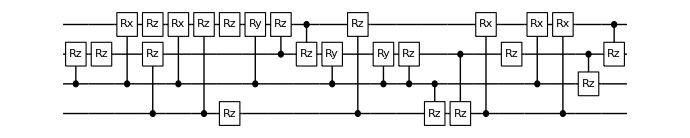

cost=8.31127×10^-7; ngates=24

runtime= 1.71009 minutes

cost=8.31127×10^-7 ;dist=0.00188231; globalphase=0.000970537

Cycle1, @Thu 17 Mar 2022 18:42:09, fev:387, <E>: 8.304199119457678e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Thu 17 Mar 2022 18:42:23, fev:475, <E>: 8.304199119457678e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Thu 17 Mar 2022 18:42:43, fev:579, <E>: 8.304199119457678e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 7}

I'm slowing down. Number of gates is increased to 70 @cycle 4

Cycle4, @Thu 17 Mar 2022 18:43:07, fev:679, <E>: 8.304199119457678e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=8.3042×10^-7

{{C_0[Rz_3[θ_1]],C_3[Rz_1[θ_13]],C_0[Rx_2[θ_15]],C_0[Ry_2[θ_16]],C_3[Ry_1[θ_17]],C_0[Rx_2[θ_20]],C_3[Rz_2[θ_21]],C_1[Rz_0[θ_28]],Rz_3[θ_27],C_0[Rz_2[θ_35]],C_1[Rz_0[θ_37]],C_0[Rz_1[θ_39]],C_1[Rz_3[θ_42]],C_0[Rz_2[θ_41]],C_0[Ry_2[θ_43]],C_2[Rz_3[θ_44]],C_3[Ry_1[θ_46]],C_0[Rz_2[θ_47]],C_1[Rz_2[θ_48]]},<|θ_1→0.00664893,θ_13→-0.0203378,θ_15→-0.185498,θ_16→-0.00293264,θ_17→0.00454118,θ_20→0.186029,θ_21→-0.00256337,θ_27→-0.0162477,θ_28→-0.413885,θ_35→-0.850401,θ_37→0.406924,θ_39→0.0138129,θ_41→0.669684,θ_42→0.0252199,θ_43→0.00293073,θ_44→0.00955218,θ_46→-0.00453987,θ_47→0.186096,θ_48→0.00665004|>,{2,3,4},733,4,{merged, θsmall, metric, bruteforce}=,{0,31,0,0},I keep failing to lower the energy. }

```mathematica
Table[
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfull2.mx",resfullH2];
,{10}];
,{t,times}];
```

```mathematica
ressubH2=<||>;
DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→50,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→0.001,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

### Subspace compilation: {0.005,0.05,0.5,2}

```mathematica
times2={0.005,0.05,0.5,2}
```

{0.005,0.05,0.5,2}

```mathematica
ressubH2<<ressubH2.mx
```

Null ressubH2

```mathematica
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→50,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→0.001,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

Cycle1, @Sat 19 Mar 2022 22:04:24, fev:403, <E>: 5.569647473224748e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:04:34, fev:490, <E>: 5.569647473224748e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:04:47, fev:585, <E>: 5.569647473224748e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 39, 5, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=5.56965×10^-7

{{C_3[Rz_0[θ_1]],C_2[Rz_1[θ_3]],C_0[Rz_3[θ_4]],Rz_3[θ_13],C_3[Rz_1[θ_16]],C_0[Rz_3[θ_38]]},<|θ_1→-0.00792821,θ_3→-0.00546393,θ_4→1.02813,θ_13→-0.00638448,θ_16→-0.00245998,θ_38→-1.01537|>,{2,3},625,3,{merged, θsmall, metric, bruteforce}=,{0,39,5,0},Compilation is either converging or stuck. }

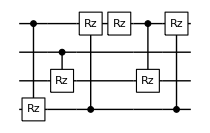

cost=5.56965×10^-7; ngates=6

runtime= 0.890364 minutes

cost=5.56965×10^-7 ;dist=0.0010084; globalphase=0.00230661

Cycle1, @Sat 19 Mar 2022 22:05:07, fev:246, <E>: 5.600907810876521e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 34, 9, 1, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:05:17, fev:333, <E>: 5.600907810876521e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 34, 9, 1, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:05:32, fev:435, <E>: 5.600907810876521e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 34, 9, 1, 3}

pruning exceeds the maxcost: 1.×10^-7; cost=5.60091×10^-7

{{Rz_0[θ_2],C_1[Rz_2[θ_20]],C_0[Rz_3[θ_15]],C_3[Rz_0[θ_25]],C_2[Rz_0[θ_32]],C_0[Rz_1[θ_41]]},<|θ_2→-0.150242,θ_15→-0.311352,θ_20→-0.311352,θ_25→0.30311,θ_32→-0.321838,θ_41→-0.319511|>,{2,3},498,3,{merged, θsmall, metric, bruteforce}=,{0,34,9,1},Compilation is either converging or stuck. }

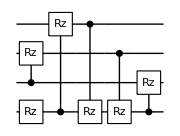

cost=5.60091×10^-7; ngates=6

runtime= 0.723097 minutes

cost=5.60091×10^-7 ;dist=0.000943637; globalphase=0.0821517

Cycle1, @Sat 19 Mar 2022 22:05:53, fev:342, <E>: 5.495147265e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 36, 8, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:06:00, fev:422, <E>: 5.495147265e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 36, 8, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:06:15, fev:531, <E>: 5.495147265e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 36, 8, 0, 4}

I'm slowing down. Number of gates is increased to 70 @cycle 4

Cycle4, @Sat 19 Mar 2022 22:06:35, fev:637, <E>: 5.495147265e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 36, 8, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=5.49515×10^-7

{{C_0[Rz_1[θ_6]],C_1[Rz_2[θ_13]],C_3[Rz_2[θ_19]],Rz_1[θ_23],C_2[Rz_3[θ_36]],C_3[Rz_1[θ_37]]},<|θ_6→-3.06219,θ_13→-1.52323,θ_19→1.53126,θ_23→2.29374,θ_36→0.0079344,θ_37→-1.5251|>,{2,3,4},687,4,{merged, θsmall, metric, bruteforce}=,{0,36,8,0},Compilation is either converging or stuck. }

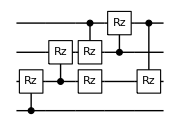

cost=5.49515×10^-7; ngates=6

runtime= 1.01337 minutes

cost=5.49515×10^-7 ;dist=0.000910131; globalphase=0.382964

Cycle1, @Sat 19 Mar 2022 22:07:09, fev:445, <E>: 6.082010042263164e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 39, 4, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:07:20, fev:542, <E>: 6.082010042263164e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 39, 4, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:07:36, fev:648, <E>: 6.082010042263164e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 39, 4, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=6.08201×10^-7

{{Rz_3[θ_12],C_0[Rz_2[θ_18]],C_1[Rz_3[θ_13]],Rz_1[θ_14],Rz_3[θ_44],C_1[Rz_0[θ_22]],C_0[Rz_3[θ_48]]},<|θ_12→-0.377513,θ_13→-0.0101668,θ_14→0.130489,θ_18→0.26963,θ_22→0.260906,θ_44→0.386747,θ_48→0.260589|>,{2,3},699,3,{merged, θsmall, metric, bruteforce}=,{0,39,4,0},Compilation is either converging or stuck. }

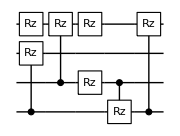

cost=6.08201×10^-7; ngates=7

runtime= 0.969255 minutes

cost=6.08201×10^-7 ;dist=0.00095238; globalphase=6.22001

Cycle1, @Sat 19 Mar 2022 22:08:04, fev:408, <E>: 5.477618267857309e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 37, 0, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:08:16, fev:503, <E>: 5.477618267857309e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 37, 0, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:08:31, fev:598, <E>: 5.477618267857309e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 37, 0, 0, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=5.47762×10^-7

{{C_1[Rz_0[θ_17]],C_0[Ry_2[θ_20]],C_1[Rz_0[θ_23]],C_0[Ry_2[θ_30]],C_2[Rz_1[θ_34]],C_2[Rx_3[θ_35]],C_0[Rz_1[θ_38]],C_1[Rz_0[θ_40]],C_2[Rx_3[θ_41]],C_0[Rz_1[θ_43]],C_2[Rz_0[θ_44]],Rz_1[θ_46]},<|θ_17→-0.311116,θ_20→-1.22221,θ_23→0.312933,θ_30→1.22221,θ_34→-0.0602304,θ_35→0.554282,θ_38→-0.32014,θ_40→0.0524103,θ_41→-0.554282,θ_43→0.205893,θ_44→-0.0621237,θ_46→0.0832646|>,{2,3},669,3,{merged, θsmall, metric, bruteforce}=,{1,37,0,0},I keep failing to lower the energy. }

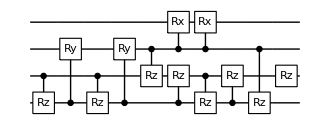

cost=5.47762×10^-7; ngates=12

runtime= 0.895586 minutes

cost=5.47762×10^-7 ;dist=0.000909792; globalphase=0.0172225

Cycle1, @Sat 19 Mar 2022 22:08:49, fev:618, <E>: 6.354660593288486e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 37, 0, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:08:58, fev:715, <E>: 6.354660593288486e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 37, 0, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:09:11, fev:813, <E>: 6.354660593288486e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 37, 0, 0, 5}

pruning exceeds the maxcost: 1.×10^-7; cost=6.35466×10^-7

{{C_0[Rz_1[θ_31]],C_0[Ry_2[θ_32]],C_0[Ry_2[θ_15]],C_2[Rz_1[θ_33]],C_1[Rz_3[θ_21]],C_2[Rz_1[θ_23]],C_0[Ry_2[θ_20]],C_3[Rz_0[θ_12]],Rz_3[θ_42],C_3[Rz_1[θ_45]],C_0[Rz_3[θ_11]],C_0[Rz_3[θ_43]]},<|θ_11→0.874838,θ_12→-0.00739099,θ_15→-1.8127,θ_20→1.1145,θ_21→-0.0816735,θ_23→-0.446288,θ_31→-0.0425534,θ_32→0.698191,θ_33→0.445663,θ_42→0.0586949,θ_43→-0.910268,θ_45→0.0364816|>,{2,3},875,3,{merged, θsmall, metric, bruteforce}=,{1,37,0,0},Compilation is either converging or stuck. }

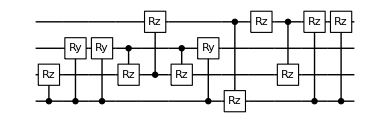

cost=6.35466×10^-7; ngates=12

runtime= 0.645422 minutes

cost=6.35466×10^-7 ;dist=0.00106183; globalphase=0.0130152

Cycle1, @Sat 19 Mar 2022 22:09:31, fev:362, <E>: 6.387978445099307e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 35, 8, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:09:42, fev:456, <E>: 6.387978445099307e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 35, 8, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:09:56, fev:556, <E>: 6.387978445099307e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 35, 8, 0, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=6.38798×10^-7

{{C_0[Rz_3[θ_17]],C_2[Rz_1[θ_9]],C_3[Ry_0[θ_18]],Rz_2[θ_27],C_1[Rz_3[θ_21]],Rz_3[θ_8],C_3[Ry_0[θ_39]]},<|θ_8→0.00592661,θ_9→0.000776693,θ_17→-0.00132164,θ_18→-0.96422,θ_21→-0.00180155,θ_27→0.00417904,θ_39→0.963648|>,{2,3},590,3,{merged, θsmall, metric, bruteforce}=,{0,35,8,0},Compilation is either converging or stuck. }

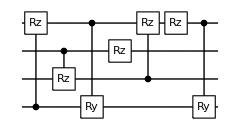

cost=6.37674×10^-7; ngates=7

runtime= 0.699918 minutes

cost=6.37674×10^-7 ;dist=0.00101905; globalphase=0.0021441

Cycle1, @Sat 19 Mar 2022 22:10:27, fev:466, <E>: 5.796094293408771e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 34, 3, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:10:40, fev:567, <E>: 5.796094293408771e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 34, 3, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:10:55, fev:661, <E>: 5.796094293408771e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 34, 3, 0, 3}

pruning exceeds the maxcost: 1.×10^-7; cost=5.79609×10^-7

{{C_0[Ry_2[θ_4]],C_0[Ry_2[θ_14]],C_0[Rz_2[θ_22]],C_0[Ry_2[θ_23]],C_0[Rx_2[θ_25]],C_0[Ry_2[θ_28]],C_0[Rz_2[θ_30]],C_3[Rz_2[θ_33]],Rz_2[θ_39],C_0[Rx_3[θ_40]],C_1[Rz_3[θ_41]],C_0[Ry_3[θ_43]],Rz_3[θ_49]},<|θ_4→-0.257477,θ_14→-1.22121,θ_22→1.09889,θ_23→2.46862,θ_25→1.80346,θ_28→-2.71761,θ_30→-0.420516,θ_33→1.85292,θ_39→-1.20373,θ_40→-3.14159,θ_41→1.2889,θ_43→3.14159,θ_49→-1.56657|>,{2,3},745,3,{merged, θsmall, metric, bruteforce}=,{0,34,3,0},Compilation is either converging or stuck. }

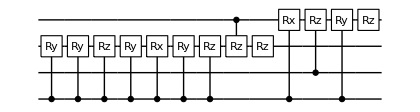

cost=5.79609×10^-7; ngates=13

runtime= 0.978547 minutes

cost=5.79609×10^-7 ;dist=0.000919557; globalphase=5.82204

Cycle1, @Sat 19 Mar 2022 22:11:25, fev:418, <E>: 5.474913734593301e-7 nansatz:8 merged-smallθ,metric,bf,gmerged: {1, 38, 3, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:11:36, fev:509, <E>: 5.474913734593301e-7 nansatz:8 merged-smallθ,metric,bf,gmerged: {1, 38, 3, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:11:50, fev:605, <E>: 5.474913734593301e-7 nansatz:8 merged-smallθ,metric,bf,gmerged: {1, 38, 3, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=5.47491×10^-7

{{C_3[Rz_0[θ_37]],C_0[Rz_3[θ_28]],C_2[Rz_0[θ_34]],C_2[Rx_3[θ_14]],C_2[Ry_3[θ_39]],C_2[Rx_3[θ_10]],C_0[Rz_2[θ_22]],Rz_0[θ_40]},<|θ_10→1.57081,θ_14→-1.57077,θ_22→0.0078911,θ_28→-0.226688,θ_34→0.224661,θ_37→0.461046,θ_39→0.234582,θ_40→-0.342854|>,{2,3},661,3,{merged, θsmall, metric, bruteforce}=,{1,38,3,0},I keep failing to lower the energy. }

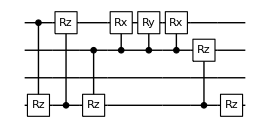

cost=5.47491×10^-7; ngates=8

runtime= 0.845835 minutes

cost=5.47491×10^-7 ;dist=0.000906284; globalphase=6.22674

Cycle1, @Sat 19 Mar 2022 22:12:11, fev:390, <E>: 6.365020706056157e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {2, 37, 3, 1, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:12:23, fev:489, <E>: 6.365020706056157e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {2, 37, 3, 1, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:12:36, fev:582, <E>: 6.365020706056157e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {2, 37, 3, 1, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=6.36502×10^-7

{{C_1[Rz_0[θ_32]],C_3[Rz_0[θ_16]],C_0[Rz_3[θ_14]],C_1[Rz_0[θ_27]],C_2[Rz_0[θ_7]],Rz_2[θ_28],C_0[Rz_3[θ_31]]},<|θ_7→0.00103031,θ_14→-0.274769,θ_16→-0.00458537,θ_27→0.653569,θ_28→0.00348059,θ_31→0.281587,θ_32→-0.651111|>,{2,3},623,3,{merged, θsmall, metric, bruteforce}=,{2,37,3,1},Compilation is either converging or stuck. }

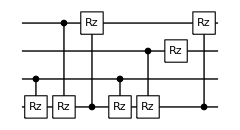

cost=6.36502×10^-7; ngates=7

runtime= 0.721125 minutes

cost=6.36502×10^-7 ;dist=0.000957666; globalphase=0.00143419

Cycle1, @Sat 19 Mar 2022 22:13:05, fev:527, <E>: 0.000054806460739964535 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 41, 4, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:13:15, fev:621, <E>: 0.000054806460739964535 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 41, 4, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:13:29, fev:724, <E>: 0.000054806460739964535 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 41, 4, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000548065

{{C_1[Rz_0[θ_6]],C_0[Rz_3[θ_7]],C_3[Rz_2[θ_10]],Rz_0[θ_41],C_2[Rz_0[θ_47]]},<|θ_6→0.00139811,θ_7→0.0775919,θ_10→0.0780303,θ_41→-0.0305523,θ_47→0.0590947|>,{2,3},747,3,{merged, θsmall, metric, bruteforce}=,{0,41,4,0},Compilation is either converging or stuck. }

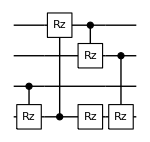

cost=0.0000548065; ngates=5

runtime= 0.869678 minutes

cost=0.0000548065 ;dist=0.00916944; globalphase=0.0021402

Cycle1, @Sat 19 Mar 2022 22:13:59, fev:511, <E>: 0.00005471643041943253 nansatz:10 merged-smallθ,metric,bf,gmerged: {1, 39, 0, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:14:09, fev:597, <E>: 0.00005471643041943253 nansatz:10 merged-smallθ,metric,bf,gmerged: {1, 39, 0, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:14:26, fev:707, <E>: 0.00005471643041943253 nansatz:10 merged-smallθ,metric,bf,gmerged: {1, 39, 0, 0, 4}

I'm slowing down. Number of gates is increased to 70 @cycle 4

Cycle4, @Sat 19 Mar 2022 22:14:44, fev:811, <E>: 0.00005471643041943253 nansatz:10 merged-smallθ,metric,bf,gmerged: {1, 39, 0, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547164

{{C_3[Ry_0[θ_48]],C_3[Ry_0[θ_18]],C_3[Rz_2[θ_16]],C_2[Rz_0[θ_3]],C_0[Rz_2[θ_28]],C_2[Rz_3[θ_8]],C_2[Rz_0[θ_33]],C_2[Rz_1[θ_12]],C_0[Rz_3[θ_9]],C_2[Rz_1[θ_20]]},<|θ_3→-0.881852,θ_8→0.0319649,θ_9→0.0631717,θ_12→0.0514367,θ_16→0.0497087,θ_18→1.641,θ_20→-0.0352418,θ_28→0.0452187,θ_33→0.897948,θ_48→-1.641|>,{2,3,4},870,4,{merged, θsmall, metric, bruteforce}=,{1,39,0,0},Compilation is either converging or stuck. }

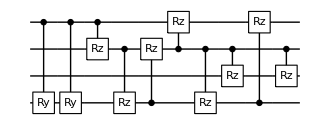

cost=0.0000547164; ngates=10

runtime= 1.22309 minutes

cost=0.0000547164 ;dist=0.00907385; globalphase=0.00158609

Cycle1, @Sat 19 Mar 2022 22:15:07, fev:382, <E>: 0.00005481947929220077 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 31, 11, 1, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:15:16, fev:470, <E>: 0.00005481947929220077 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 31, 11, 1, 5}

Cycle3, @Sat 19 Mar 2022 22:15:53, fev:969, <E>: 0.00005472337166423369 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 53, 18, 1, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Sat 19 Mar 2022 22:16:10, fev:1066, <E>: 0.00005472337166423369 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 53, 18, 1, 9}

I'm slowing down. Number of gates is increased to 70 @cycle 5

Cycle5, @Sat 19 Mar 2022 22:16:35, fev:1185, <E>: 0.00005472337166423369 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 53, 18, 1, 12}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547234

{{Ry_1[θ_65],C_0[Rz_3[θ_83]],Rz_0[θ_25],C_1[Rz_2[θ_89]],C_0[Rz_1[θ_97]],C_1[Rz_0[θ_54]],C_1[Rz_3[θ_55]],Rz_3[θ_52],C_1[Rz_0[θ_69]],C_2[Rz_0[θ_30]],Ry_1[θ_74],C_3[Rz_0[θ_76]],C_0[Rz_1[θ_66]],C_2[Rz_1[θ_5]],C_2[Ry_1[θ_56]],C_1[Rz_3[θ_75]],Rx_1[θ_16],C_1[Rz_0[θ_57]],C_2[Rx_1[θ_59]],C_0[Rz_1[θ_91]],Rz_2[θ_87],C_0[Ry_1[θ_10]],C_2[Rz_1[θ_96]],Rz_1[θ_86],Rx_1[θ_42]},<|θ_5→0.0755147,θ_10→-0.775316,θ_16→2.10831,θ_25→-0.246311,θ_30→-0.483811,θ_42→-2.06076,θ_52→0.0326151,θ_54→0.791915,θ_55→-0.318556,θ_56→0.305613,θ_57→-0.78946,θ_59→0.360247,θ_65→-0.00102568,θ_66→-1.39501,θ_69→0.673657,θ_74→0.401544,θ_75→-0.000471557,θ_76→-0.909759,θ_83→-0.672201,θ_86→-0.853074,θ_87→-0.776236,θ_89→0.421404,θ_91→0.524771,θ_96→-0.469694,θ_97→-1.37626|>,{2,4,5},1350,5,{merged, θsmall, metric, bruteforce}=,{0,53,18,1},Compilation is either converging or stuck. }

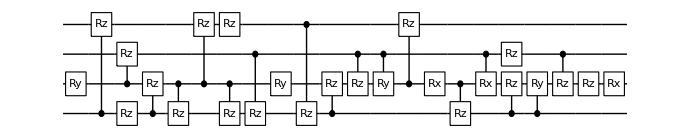

cost=0.0000547234; ngates=25

runtime= 1.84651 minutes

cost=0.0000547234 ;dist=0.00907719; globalphase=0.217606

Cycle1, @Sat 19 Mar 2022 22:17:04, fev:389, <E>: 0.000054768379397884814 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 33, 10, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:17:14, fev:477, <E>: 0.000054768379397884814 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 33, 10, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:17:30, fev:584, <E>: 0.000054768379397884814 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 33, 10, 0, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547684

{{Rz_1[θ_2],C_0[Ry_1[θ_24]],C_0[Rz_1[θ_12]],C_0[Rz_3[θ_25]],C_0[Ry_1[θ_16]],C_1[Rz_3[θ_5]],C_3[Rz_0[θ_27]]},<|θ_2→-0.0250058,θ_5→-0.0484197,θ_12→-0.0282599,θ_16→-0.014769,θ_24→0.0145768,θ_25→0.0486065,θ_27→-0.0789535|>,{2,3},620,3,{merged, θsmall, metric, bruteforce}=,{0,33,10,0},Compilation is either converging or stuck. }

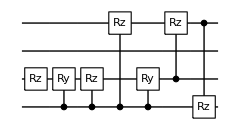

cost=0.0000547684; ngates=7

runtime= 0.817263 minutes

cost=0.0000547684 ;dist=0.00910143; globalphase=0.0290219

Cycle1, @Sat 19 Mar 2022 22:17:59, fev:417, <E>: 0.0000547133837371927 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 40, 4, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:18:09, fev:513, <E>: 0.0000547133837371927 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 40, 4, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:18:22, fev:612, <E>: 0.0000547133837371927 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 40, 4, 0, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547134

{{Rz_0[θ_9],Rz_2[θ_22],Rz_3[θ_27],C_1[Rz_0[θ_14]],C_3[Rz_0[θ_32]]},<|θ_9→-0.0192553,θ_14→0.0203799,θ_22→0.0394855,θ_27→0.0394854,θ_32→0.0181307|>,{2,3},631,3,{merged, θsmall, metric, bruteforce}=,{1,40,4,0},I keep failing to lower the energy. }

-Graphics-

cost=0.0000547134; ngates=5

runtime= 0.82777 minutes

cost=0.0000547134 ;dist=0.00906049; globalphase=0.0169158

Cycle1, @Sat 19 Mar 2022 22:18:43, fev:317, <E>: 0.000054789596514281946 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 36, 8, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:18:51, fev:391, <E>: 0.000054789596514281946 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 36, 8, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:19:02, fev:474, <E>: 0.000054789596514281946 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 36, 8, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547896

{{C_1[Rz_0[θ_6]],C_3[Rz_0[θ_14]],C_0[Rz_1[θ_15]],Rz_0[θ_31],C_2[Rz_1[θ_34]]},<|θ_6→0.546446,θ_14→-0.426544,θ_15→-0.525189,θ_31→-0.0995628,θ_34→0.445927|>,{2,3},531,3,{merged, θsmall, metric, bruteforce}=,{1,36,8,0},Compilation is either converging or stuck. }

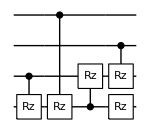

cost=0.0000547896; ngates=5

runtime= 0.658081 minutes

cost=0.0000547896 ;dist=0.00915378; globalphase=0.0169165

Cycle1, @Sat 19 Mar 2022 22:19:19, fev:305, <E>: 0.00005480933994328474 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 30, 10, 2, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:19:30, fev:401, <E>: 0.00005480933994328474 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 30, 10, 2, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:19:40, fev:495, <E>: 0.00005480933994328474 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 30, 10, 2, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000548093

{{C_2[Rz_0[θ_46]],Rz_2[θ_19],C_1[Rz_0[θ_13]],C_0[Rz_3[θ_11]],C_1[Rz_0[θ_12]],C_3[Rz_0[θ_37]],C_0[Rz_2[θ_1]]},<|θ_1→1.7027,θ_11→0.0776201,θ_12→-0.215985,θ_13→0.816825,θ_19→-0.812373,θ_37→0.520717,θ_46→-1.12266|>,{2,3},551,3,{merged, θsmall, metric, bruteforce}=,{0,30,10,2},Compilation is either converging or stuck. }

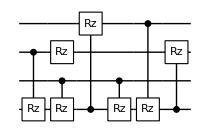

cost=0.0000548093; ngates=7

runtime= 0.619345 minutes

cost=0.0000548093 ;dist=0.00912913; globalphase=6.15509

Cycle1, @Sat 19 Mar 2022 22:20:12, fev:559, <E>: 0.00005479070760050497 nansatz:6 merged-smallθ,metric,bf,gmerged: {2, 39, 0, 3, 8}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:20:23, fev:652, <E>: 0.00005479070760050497 nansatz:6 merged-smallθ,metric,bf,gmerged: {2, 39, 0, 3, 9}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:20:34, fev:741, <E>: 0.00005479070760050497 nansatz:6 merged-smallθ,metric,bf,gmerged: {2, 39, 0, 3, 11}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547907

{{C_1[Rz_0[θ_5]],C_2[Rz_0[θ_7]],Rz_1[θ_12],C_0[Rz_1[θ_13]],C_2[Rz_1[θ_16]],C_2[Rz_3[θ_26]]},<|θ_5→-0.489481,θ_7→0.410856,θ_12→-0.714104,θ_13→0.919735,θ_16→0.429747,θ_26→0.000999916|>,{2,3},777,3,{merged, θsmall, metric, bruteforce}=,{2,39,0,3},Compilation is either converging or stuck. }

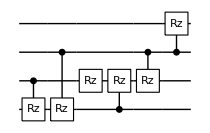

cost=0.0000547907; ngates=6

runtime= 0.84618 minutes

cost=0.0000547907 ;dist=0.00924715; globalphase=6.19739

Cycle1, @Sat 19 Mar 2022 22:20:56, fev:403, <E>: 0.00005474319275211581 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 41, 4, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:21:06, fev:501, <E>: 0.00005474319275211581 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 41, 4, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:21:20, fev:598, <E>: 0.00005474319275211581 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 41, 4, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547432

{{C_3[Rz_0[θ_7]],C_1[Rz_2[θ_15]],C_1[Rz_0[θ_22]],C_0[Rz_3[θ_25]],Rz_3[θ_31]},<|θ_7→-0.0196301,θ_15→0.0790128,θ_22→0.0196773,θ_25→-0.0419424,θ_31→0.0603534|>,{2,3},629,3,{merged, θsmall, metric, bruteforce}=,{0,41,4,0},Compilation is either converging or stuck. }

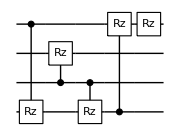

cost=0.0000547432; ngates=5

runtime= 0.758718 minutes

cost=0.0000547432 ;dist=0.00906251; globalphase=0.016917

Cycle1, @Sat 19 Mar 2022 22:21:44, fev:381, <E>: 0.0000547157389083619 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 28, 9, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:21:59, fev:490, <E>: 0.0000547157389083619 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 28, 9, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:22:15, fev:591, <E>: 0.0000547157389083619 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 28, 9, 0, 12}

Cycle4, @Sat 19 Mar 2022 22:23:04, fev:1173, <E>: 5.036743611075423e-8 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 85, 9, 0, 19}

{{C_2[Rx_0[θ_63]],C_2[Rz_1[θ_2]],C_1[Rx_2[θ_87]],C_1[Rx_3[θ_58]],C_3[Rz_1[θ_105]],C_0[Rx_1[θ_75]],C_1[Rx_3[θ_4]],C_1[Rx_2[θ_97]],C_2[Rx_0[θ_70]],C_1[Rz_0[θ_20]],C_3[Rz_2[θ_17]],Rz_3[θ_90],Rz_1[θ_31]},<|θ_2→0.0181176,θ_4→-3.14159,θ_17→0.0496622,θ_20→-0.0293014,θ_31→3.92623,θ_58→3.14159,θ_63→3.17023,θ_70→-3.17023,θ_75→0.0182521,θ_87→3.1416,θ_90→2.35815,θ_97→-3.1416,θ_105→4.66664|>,{2,3},1268,4,{merged, θsmall, metric, bruteforce}=,{0,85,9,0},Circuit within target precision is found}

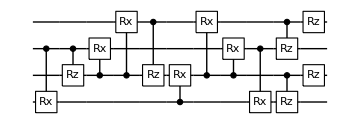

cost=5.03674×10^-8; ngates=13

runtime= 1.76359 minutes

cost=5.03674×10^-8 ;dist=0.00036617; globalphase=3.15851

Cycle1, @Sat 19 Mar 2022 22:23:42, fev:511, <E>: 0.005322543273934777 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 42, 0, 2, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:23:51, fev:592, <E>: 0.005322543273934777 nansatz:5 merged-smallθ,metric,bf,gmerged: {1, 42, 0, 2, 3}

Cycle3, @Sat 19 Mar 2022 22:24:25, fev:1064, <E>: 0.0002243882884166437 nansatz:14 merged-smallθ,metric,bf,gmerged: {1, 81, 0, 2, 5}

{{C_0[Rz_3[θ_1]],C_2[Rz_1[θ_33]],C_1[Rx_2[θ_58]],C_0[Rx_1[θ_65]],C_3[Rz_2[θ_141]],C_0[Rx_3[θ_66]],Ry_0[θ_126],C_1[Ry_0[θ_76]],C_3[Ry_0[θ_137]],C_0[Rx_3[θ_132]],C_1[Rz_3[θ_130]],C_0[Rx_1[θ_87]],C_1[Rx_2[θ_89]],C_2[Rz_3[θ_115]],C_2[Rz_0[θ_110]],C_3[Rz_1[θ_95]],C_3[Rz_2[θ_111]],C_3[Rz_0[θ_100]]},<|θ_1→6.33694,θ_33→2.79996,θ_58→-3.14159,θ_65→3.14159,θ_66→-3.14159,θ_76→-0.176378,θ_87→-3.14159,θ_89→3.14159,θ_95→-7.33134,θ_100→-6.87,θ_110→5.87737,θ_111→-1.84057,θ_115→0.590747,θ_126→-0.00482917,θ_130→1.89909,θ_132→3.14159,θ_137→0.181208,θ_141→3.5392|>,{2},2032,4,{merged, θsmall, metric, bruteforce}=,{1,119,6,2},Circuit within target precision is found}

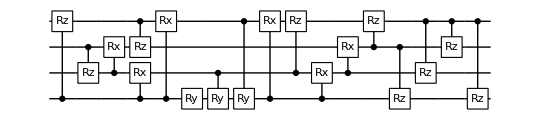

cost=2.90723×10^-8; ngates=18

runtime= 1.92705 minutes

cost=2.90723×10^-8 ;dist=0.000248536; globalphase=3.67413

Cycle1, @Sat 19 Mar 2022 22:25:44, fev:671, <E>: 0.0053225042250808485 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 3}

Cycle2, @Sat 19 Mar 2022 22:26:12, fev:1048, <E>: 0.00020537193118996822 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 69, 8, 0, 7}

{{C_2[Rz_1[θ_62]],Rz_0[θ_12],C_3[Rz_1[θ_116]],C_3[Rx_2[θ_10]],C_3[Ry_1[θ_120]],Rz_1[θ_97],C_0[Rx_3[θ_57]],C_2[Ry_0[θ_91]],Ry_0[θ_126],C_1[Ry_0[θ_67]],C_0[Rx_3[θ_61]],C_3[Rx_2[θ_4]],C_3[Rz_0[θ_5]],C_3[Rz_1[θ_100]],C_3[Ry_1[θ_81]]},<|θ_4→3.14159,θ_5→-3.53911,θ_10→-3.14159,θ_12→1.37364,θ_57→-3.14159,θ_61→3.14159,θ_62→3.51613,θ_67→-0.181232,θ_81→-3.14159,θ_91→-0.00470446,θ_97→-2.05245,θ_100→0.395098,θ_116→-3.91285,θ_120→3.14159,θ_126→0.00470397|>,{},1876,3,{merged, θsmall, metric, bruteforce}=,{0,106,8,0},Circuit within target precision is found}

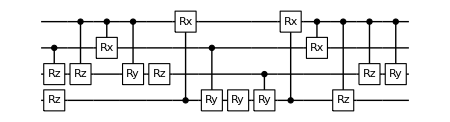

cost=5.84349×10^-8; ngates=15

runtime= 1.97147 minutes

cost=5.84349×10^-8 ;dist=0.000339167; globalphase=0.22003

Cycle1, @Sat 19 Mar 2022 22:27:37, fev:462, <E>: 0.005322493883759161 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 3, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:27:51, fev:566, <E>: 0.005322493883759161 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 3, 4}

Cycle3, @Sat 19 Mar 2022 22:28:32, fev:1124, <E>: 0.001939295751724024 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 74, 8, 3, 4}

{{C_0[Rz_2[θ_8]],C_0[Ry_3[θ_56]],C_1[Ry_0[θ_63]],C_2[Rz_0[θ_126]],C_2[Ry_1[θ_82]],C_1[Rx_2[θ_131]],C_0[Rz_2[θ_139]],C_0[Ry_2[θ_123]],C_0[Rz_2[θ_137]],Rx_2[θ_105],C_0[Rz_3[θ_125]],C_2[Ry_1[θ_69]],C_2[Rz_0[θ_109]],C_1[Rx_0[θ_67]],C_3[Rz_2[θ_34]],C_2[Rz_3[θ_100]],C_0[Rx_3[θ_51]]},<|θ_8→-2.74544,θ_34→-0.464271,θ_51→-3.14159,θ_56→3.14159,θ_63→-3.14159,θ_67→-3.14159,θ_69→-3.14159,θ_82→-3.14159,θ_100→3.60696,θ_105→0.00460016,θ_109→-4.39404,θ_123→-0.178284,θ_125→1.04943,θ_126→2.74476,θ_131→-0.181143,θ_137→2.44879,θ_139→-1.59042|>,{2},2231,4,{merged, θsmall, metric, bruteforce}=,{0,112,13,4},Circuit within target precision is found}

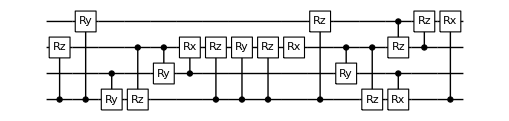

cost=8.97706×10^-8; ngates=17

runtime= 2.24926 minutes

cost=8.97706×10^-8 ;dist=0.000339898; globalphase=5.30555

{{C_2[Ry_1[θ_24]],C_3[Rx_0[θ_25]],C_2[Ry_1[θ_14]],C_0[Rz_3[θ_17]],C_1[Ry_2[θ_23]],C_1[Ry_2[θ_8]],C_1[Ry_2[θ_36]],C_3[Ry_1[θ_43]],C_3[Rx_2[θ_41]],Rz_1[θ_47],C_1[Rx_3[θ_32]],C_2[Rz_3[θ_9]],C_2[Rz_0[θ_13]],C_1[Ry_3[θ_3]],C_3[Ry_0[θ_28]],C_3[Rx_2[θ_10]],C_3[Rx_1[θ_26]],C_3[Ry_1[θ_46]],C_3[Rx_2[θ_31]],C_2[Rz_0[θ_48]],C_3[Rx_1[θ_27]]},<|θ_3→-0.00443528,θ_8→0.953804,θ_9→1.36023,θ_10→2.69291,θ_13→-3.11922,θ_14→0.098041,θ_17→-2.72045,θ_23→-0.00105971,θ_24→-0.0980405,θ_25→3.14159,θ_26→4.71259,θ_27→-1.57144,θ_28→3.14159,θ_31→0.448684,θ_32→-0.176672,θ_36→-0.952744,θ_41→-3.14159,θ_43→-3.14211,θ_46→-0.989172,θ_47→-3.39966,θ_48→-1.73127|>,{},607,1,{merged, θsmall, metric, bruteforce}=,{0,29,0,0},Circuit within target precision is found}

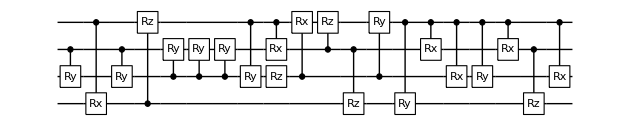

cost=7.9745×10^-8; ngates=21

runtime= 0.635558 minutes

cost=7.9745×10^-8 ;dist=0.000475169; globalphase=0.220088

Cycle1, @Sat 19 Mar 2022 22:30:38, fev:519, <E>: 6.54659489174314e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 30, 5, 0, 5}

{{C_0[Ry_1[θ_5]],C_2[Ry_0[θ_7]],C_0[Rz_2[θ_13]],C_2[Rx_3[θ_14]],C_0[Ry_2[θ_90]],C_3[Rz_2[θ_19]],C_1[Rz_2[θ_59]],C_0[Ry_2[θ_24]],C_2[Rx_3[θ_34]],C_1[Rz_0[θ_27]],C_2[Rz_1[θ_62]],C_2[Ry_0[θ_40]],C_0[Ry_1[θ_49]],C_3[Rz_2[θ_64]],C_1[Rz_0[θ_63]],C_0[Rz_2[θ_50]]},<|θ_5→-3.14159,θ_7→3.14159,θ_13→0.395339,θ_14→-3.14159,θ_19→-0.101335,θ_24→-0.251474,θ_27→0.582554,θ_34→3.14159,θ_40→-3.14159,θ_49→3.14159,θ_50→0.983523,θ_59→-0.181008,θ_62→-0.511734,θ_63→0.397623,θ_64→-0.305067,θ_90→0.0746729|>,{},1164,2,{merged, θsmall, metric, bruteforce}=,{0,62,12,0},Circuit within target precision is found}

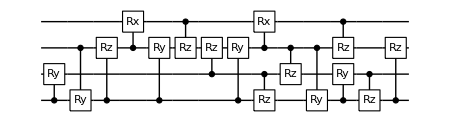

cost=4.4346×10^-8; ngates=16

runtime= 1.15338 minutes

cost=4.4346×10^-8 ;dist=0.000353926; globalphase=0.0689141

Cycle1, @Sat 19 Mar 2022 22:31:47, fev:419, <E>: 0.0051300039483812565 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 0}

Cycle2, @Sat 19 Mar 2022 22:32:25, fev:968, <E>: 0.0004829351064946641 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 71, 1, 0, 1}

{{C_3[Rz_0[θ_47]],C_1[Rx_0[θ_4]],C_1[Rz_0[θ_57]],C_2[Rz_0[θ_104]],C_0[Rz_2[θ_114]],C_1[Rx_2[θ_1]],C_1[Ry_3[θ_42]],C_3[Rz_1[θ_75]],Rx_1[θ_73],C_0[Rx_1[θ_105]],C_1[Ry_0[θ_124]],C_1[Rz_0[θ_89]],C_1[Ry_0[θ_113]],C_2[Ry_1[θ_28]],C_1[Rx_2[θ_26]],C_3[Rz_2[θ_115]],C_1[Ry_3[θ_25]],C_1[Rx_0[θ_7]],C_2[Rz_1[θ_82]],C_1[Ry_3[θ_117]]},<|θ_1→-3.14159,θ_4→-3.14159,θ_7→3.14159,θ_25→3.16259,θ_26→3.14159,θ_28→0.181219,θ_42→-3.14159,θ_47→-2.563,θ_57→0.679479,θ_73→-0.00468663,θ_75→-3.04395,θ_82→2.74439,θ_89→-3.14048,θ_104→2.25744,θ_105→0.185911,θ_113→-0.00153531,θ_114→0.294601,θ_115→0.197573,θ_117→-0.0210003,θ_124→-0.00153526|>,{},1812,3,{merged, θsmall, metric, bruteforce}=,{0,109,1,0},Circuit within target precision is found}

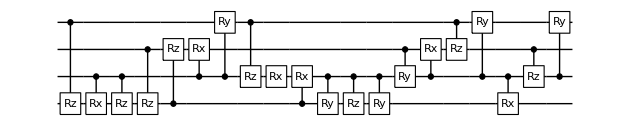

cost=1.19052×10^-8; ngates=20

runtime= 2.0374 minutes

cost=1.19052×10^-8 ;dist=0.00016927; globalphase=0.169153

Cycle1, @Sat 19 Mar 2022 22:33:57, fev:442, <E>: 0.005322498915805163 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 27, 0, 0, 3}

Cycle2, @Sat 19 Mar 2022 22:34:26, fev:806, <E>: 0.00046411172208771223 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 65, 11, 0, 3}

Cycle3, @Sat 19 Mar 2022 22:34:52, fev:1274, <E>: 0.00003713361991619646 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 102, 14, 0, 4}

Cycle4, @Sat 19 Mar 2022 22:35:21, fev:1783, <E>: 2.198192273761279e-6 nansatz:14 merged-smallθ,metric,bf,gmerged: {1, 135, 19, 0, 6}

Cycle5, @Sat 19 Mar 2022 22:35:50, fev:2146, <E>: 5.517709844582441e-9 nansatz:15 merged-smallθ,metric,bf,gmerged: {2, 166, 24, 2, 7}

{{C_0[Rx_3[θ_114]],C_3[Rz_1[θ_116]],Rz_3[θ_200],C_0[Ry_1[θ_53]],C_2[Rx_0[θ_54]],C_3[Rx_2[θ_203]],C_1[Rx_2[θ_208]],C_0[Rx_2[θ_60]],C_2[Rx_0[θ_89]],C_3[Rz_2[θ_206]],C_0[Ry_1[θ_74]],C_0[Rx_3[θ_67]],Rz_1[θ_148],C_3[Rz_0[θ_36]],C_0[Rz_2[θ_165]]},<|θ_36→-0.791788,θ_53→-3.14159,θ_54→3.14159,θ_60→-0.178875,θ_67→-3.14159,θ_74→3.14159,θ_89→-3.14159,θ_114→3.14159,θ_116→-0.396015,θ_148→-0.293859,θ_165→-0.204014,θ_200→-0.384494,θ_203→0.0023357,θ_206→-0.191993,θ_208→-0.00233547|>,{},2223,5,{merged, θsmall, metric, bruteforce}=,{2,166,24,2},Circuit within target precision is found}

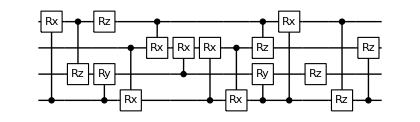

cost=5.51771×10^-9; ngates=15

runtime= 2.46582 minutes

cost=5.51771×10^-9 ;dist=0.0000926686; globalphase=0.220164

Cycle1, @Sat 19 Mar 2022 22:36:24, fev:531, <E>: 9.311615922769079e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 32, 2, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:36:39, fev:631, <E>: 9.311615922769079e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 32, 2, 0, 7}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:36:57, fev:734, <E>: 9.311615922769079e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 32, 2, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=9.31162×10^-7

{{Rz_1[θ_31],C_0[Rz_1[θ_36]],C_3[Ry_0[θ_47]],C_1[Rz_2[θ_39]],Rz_0[θ_25],C_3[Ry_2[θ_33]],C_3[Ry_1[θ_5]],C_1[Ry_3[θ_41]],C_3[Ry_2[θ_6]],Rz_2[θ_28],Rz_3[θ_48],C_3[Ry_0[θ_13]],C_3[Ry_1[θ_16]],C_0[Rz_2[θ_35]],C_1[Rz_0[θ_4]],Rz_2[θ_26]},<|θ_4→-0.396449,θ_5→-3.14094,θ_6→-3.14159,θ_13→3.14159,θ_16→3.14071,θ_25→-1.22821,θ_26→0.562989,θ_28→1.24264,θ_31→-0.262982,θ_33→3.14159,θ_35→-0.470584,θ_36→0.129422,θ_39→-2.74563,θ_41→-0.178851,θ_47→-3.14159,θ_48→0.197639|>,{2,3},892,3,{merged, θsmall, metric, bruteforce}=,{0,32,2,0},Compilation is either converging or stuck. }

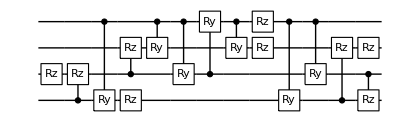

cost=9.31162×10^-7; ngates=16

runtime= 1.14499 minutes

cost=9.31162×10^-7 ;dist=0.00125139; globalphase=0.286812

Cycle1, @Sat 19 Mar 2022 22:37:28, fev:460, <E>: 0.005322537718250531 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:37:38, fev:556, <E>: 0.005322537718250531 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:37:50, fev:642, <E>: 0.005322537718250531 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.00532254

{{C_3[Rz_1[θ_3]],C_0[Rz_3[θ_28]],Rz_3[θ_29],C_1[Rz_0[θ_38]],C_2[Rz_1[θ_41]],C_0[Rz_2[θ_49]]},<|θ_3→-0.996063,θ_28→-1.01837,θ_29→0.711008,θ_38→-0.387924,θ_41→0.607437,θ_49→0.403814|>,{2,3},714,3,{merged, θsmall, metric, bruteforce}=,{0,38,6,0},Compilation is either converging or stuck. }

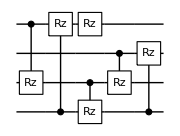

cost=0.00532254; ngates=6

runtime= 0.782223 minutes

cost=0.00532254 ;dist=0.0905743; globalphase=0.317091

Cycle1, @Sat 19 Mar 2022 22:38:21, fev:412, <E>: 0.003703924788871382 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 37, 1, 0, 3}

Cycle2, @Sat 19 Mar 2022 22:39:16, fev:1266, <E>: 0.0009349698175148413 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 66, 5, 0, 5}

Cycle3, @Sat 19 Mar 2022 22:40:56, fev:2505, <E>: 0.00008288416705959367 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 100, 10, 0, 6}

Cycle4, @Sat 19 Mar 2022 22:42:15, fev:3386, <E>: 1.6098029875788455e-6 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 131, 22, 0, 7}

{{C_1[Rz_3[θ_188]],C_3[Rz_1[θ_201]],C_0[Rx_3[θ_33]],C_2[Ry_0[θ_2]],Rz_3[θ_62],C_2[Rz_0[θ_101]],C_2[Rx_1[θ_170]],C_3[Rz_2[θ_54]],C_0[Rx_2[θ_193]],C_2[Rz_3[θ_63]],C_0[Ry_2[θ_126]],C_2[Rz_1[θ_205]],C_2[Ry_0[θ_8]],C_2[Ry_1[θ_165]],C_0[Rx_3[θ_50]]},<|θ_2→3.14159,θ_8→-3.14159,θ_33→3.14159,θ_50→-3.14159,θ_54→-5.22498,θ_62→1.44386,θ_63→6.16709,θ_101→-0.27256,θ_126→2.96617,θ_165→3.14159,θ_170→9.42478,θ_188→-2.19658,θ_193→3.17663,θ_201→1.72031,θ_205→-5.89072|>,{},4179,5,{merged, θsmall, metric, bruteforce}=,{0,162,31,0},Circuit within target precision is found}

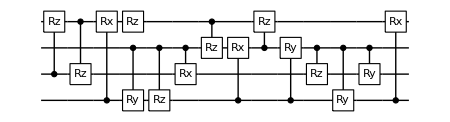

cost=2.6637×10^-8; ngates=15

runtime= 5.01679 minutes

cost=2.6637×10^-8 ;dist=0.000214019; globalphase=3.36168

Cycle1, @Sat 19 Mar 2022 22:43:14, fev:414, <E>: 0.05924738304807575 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 30, 6, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:43:22, fev:497, <E>: 0.05924738304807575 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 30, 6, 0, 3}

Cycle3, @Sat 19 Mar 2022 22:44:18, fev:1311, <E>: 0.019380704941599824 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 60, 15, 0, 6}

{{C_2[Rz_0[θ_107]],C_3[Ry_2[θ_76]],C_3[Rz_1[θ_120]],C_3[Ry_0[θ_130]],C_3[Ry_0[θ_108]],C_3[Rz_2[θ_121]],C_3[Rx_0[θ_137]],C_3[Ry_1[θ_54]],Ry_3[θ_94],C_1[Rz_3[θ_116]],C_2[Ry_3[θ_68]],Rz_1[θ_85],C_3[Rx_2[θ_134]],C_3[Ry_2[θ_98]],C_3[Rz_2[θ_103]],C_3[Ry_2[θ_114]],C_3[Ry_1[θ_42]],C_1[Rz_0[θ_86]],Rz_3[θ_139],C_3[Ry_0[θ_78]]},<|θ_42→3.14159,θ_54→-3.14159,θ_68→-0.450839,θ_76→-3.14159,θ_78→3.14159,θ_85→-0.212522,θ_86→-1.05126,θ_94→0.451032,θ_98→3.14419,θ_103→-8.28506,θ_107→-0.950044,θ_108→0.22924,θ_114→0.00622184,θ_116→1.90278,θ_120→-2.29005,θ_121→-0.0014812,θ_130→-0.22924,θ_134→-0.00564887,θ_137→-3.14159,θ_139→-1.37559|>,{2},2477,4,{merged, θsmall, metric, bruteforce}=,{0,108,15,0},Circuit within target precision is found}

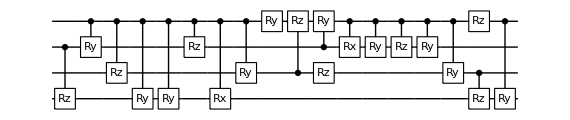

cost=8.82211×10^-8; ngates=20

runtime= 2.75748 minutes

cost=8.82211×10^-8 ;dist=0.000374249; globalphase=1.38041

Cycle1, @Sat 19 Mar 2022 22:46:02, fev:718, <E>: 0.03830372332728105 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 36, 2, 0, 0}

{{C_2[Rz_3[θ_5]],C_0[Rz_2[θ_13]],C_2[Rz_1[θ_54]],C_3[Rx_0[θ_16]],C_3[Ry_2[θ_21]],C_3[Rx_1[θ_33]],C_2[Rx_3[θ_35]],C_1[Ry_3[θ_63]],C_0[Rz_2[θ_39]],C_1[Rz_3[θ_70]],C_1[Rx_3[θ_80]],C_1[Rz_0[θ_73]],C_2[Rx_3[θ_81]],C_3[Rx_1[θ_44]],C_3[Rx_0[θ_46]],C_3[Ry_2[θ_48]]},<|θ_5→7.44248,θ_13→-3.09018,θ_16→3.14159,θ_21→-3.14159,θ_33→-3.14159,θ_35→0.506854,θ_39→6.79999,θ_44→3.14159,θ_46→-9.42478,θ_48→-3.14159,θ_54→2.03355,θ_63→0.77179,θ_70→2.24351,θ_73→-2.40086,θ_80→0.675297,θ_81→-0.506667|>,{},1229,2,{merged, θsmall, metric, bruteforce}=,{0,66,8,0},Circuit within target precision is found}

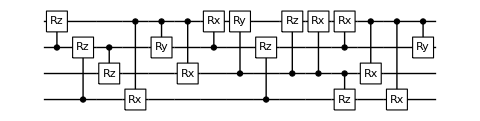

cost=3.49679×10^-8; ngates=16

runtime= 0.749717 minutes

cost=3.49679×10^-8 ;dist=0.000295452; globalphase=4.46159

Cycle1, @Sat 19 Mar 2022 22:47:08, fev:701, <E>: 0.0031308310507909276 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 33, 3, 0, 2}

Cycle2, @Sat 19 Mar 2022 22:47:46, fev:1336, <E>: 5.120619607446031e-6 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 65, 9, 0, 2}

{{C_3[Rz_2[θ_125]],Rz_1[θ_101],C_2[Ry_3[θ_3]],C_3[Rz_1[θ_122]],C_1[Rz_0[θ_96]],C_2[Rx_0[θ_16]],C_2[Rx_1[θ_32]],C_3[Ry_2[θ_81]],C_2[Rz_3[θ_74]],C_1[Rx_2[θ_69]],C_0[Rx_2[θ_39]],C_0[Rz_3[θ_99]],C_2[Ry_3[θ_40]],C_3[Rz_1[θ_44]],C_2[Ry_0[θ_119]],C_1[Rz_0[θ_100]],C_2[Rx_1[θ_45]]},<|θ_3→-3.14159,θ_16→3.14159,θ_32→3.14159,θ_39→0.587658,θ_40→-3.14159,θ_44→-3.14331,θ_45→-3.14159,θ_69→-0.137325,θ_74→3.15004,θ_81→-0.137295,θ_96→-3.20862,θ_99→-5.55995,θ_100→-1.62227,θ_101→-2.35623,θ_119→-3.14159,θ_122→-0.058934,θ_125→-1.52797|>,{},2006,3,{merged, θsmall, metric, bruteforce}=,{0,97,13,2},Circuit within target precision is found}

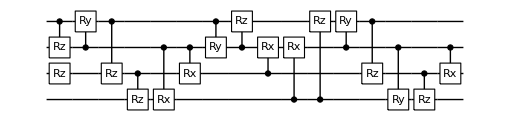

cost=8.92422×10^-8; ngates=17

runtime= 1.89219 minutes

cost=8.92422×10^-8 ;dist=0.000362664; globalphase=1.46198

Cycle1, @Sat 19 Mar 2022 22:48:56, fev:546, <E>: 0.0020882127208041723 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 30, 3, 0, 1}

{{C_0[Rz_3[θ_1]],C_1[Rx_0[θ_3]],C_3[Rz_2[θ_7]],C_3[Rx_2[θ_9]],C_1[Rx_3[θ_10]],C_0[Ry_1[θ_79]],C_3[Rz_1[θ_71]],C_3[Rx_1[θ_67]],C_0[Ry_1[θ_16]],C_1[Ry_3[θ_22]],C_3[Rx_2[θ_26]],C_1[Rx_0[θ_43]],Rz_0[θ_58],Rz_1[θ_76],C_2[Rz_3[θ_70]],C_2[Rz_1[θ_50]]},<|θ_1→6.72521,θ_3→3.14159,θ_7→3.11411,θ_9→-3.14159,θ_10→-3.14159,θ_16→2.36399,θ_22→-3.14159,θ_26→3.14159,θ_43→-3.14159,θ_50→-9.14191,θ_58→1.29845,θ_67→-0.450472,θ_70→-5.44081,θ_71→-7.69747,θ_76→2.07184,θ_79→-2.36388|>,{},1793,2,{merged, θsmall, metric, bruteforce}=,{0,68,6,0},Circuit within target precision is found}

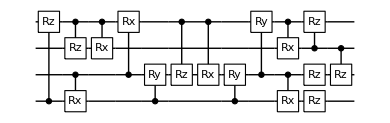

cost=2.55043×10^-8; ngates=16

runtime= 1.79823 minutes

cost=2.55043×10^-8 ;dist=0.000263187; globalphase=4.60362

Cycle1, @Sat 19 Mar 2022 22:50:51, fev:793, <E>: 0.0020883145107336576 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 28, 5, 0, 2}

{{Rz_3[θ_70],C_2[Rz_1[θ_21]],C_1[Rz_2[θ_27]],C_3[Rz_1[θ_78]],C_2[Ry_0[θ_7]],C_3[Rz_1[θ_23]],C_0[Rz_1[θ_75]],C_0[Rz_1[θ_77]],C_0[Rz_2[θ_71]],C_2[Ry_1[θ_32]],C_0[Rz_3[θ_72]],Rz_2[θ_29],C_2[Rz_0[θ_10]],C_2[Rz_3[θ_54]],C_0[Rz_2[θ_89]],Rz_3[θ_79],C_1[Rz_2[θ_57]],C_0[Ry_2[θ_17]],C_0[Rz_1[θ_83]],C_2[Rx_3[θ_26]],C_0[Rx_2[θ_28]],C_0[Ry_2[θ_20]],C_2[Rz_1[θ_19]],C_0[Rx_2[θ_65]],C_1[Rz_3[θ_62]],C_2[Ry_1[θ_43]],C_3[Rz_1[θ_67]],C_1[Rz_0[θ_80]],C_2[Rx_0[θ_39]],C_0[Rx_3[θ_44]],Rz_2[θ_33],C_1[Rz_0[θ_53]],C_1[Rz_3[θ_87]],C_3[Rz_1[θ_86]]},<|θ_7→3.14159,θ_10→-0.172374,θ_17→-3.14159,θ_19→1.06387,θ_20→2.6721,θ_21→-3.65553,θ_23→1.95662,θ_26→3.14159,θ_27→5.59011,θ_28→-0.998086,θ_29→-3.57825,θ_32→-3.14159,θ_33→0.704506,θ_39→-3.14159,θ_43→3.1416,θ_44→-3.14159,θ_53→-0.470547,θ_54→-0.617029,θ_57→0.936106,θ_62→0.422928,θ_65→-0.654841,θ_67→-0.519251,θ_70→0.393613,θ_71→0.824825,θ_72→-1.01618,θ_75→0.128716,θ_77→-0.170169,θ_78→0.132431,θ_79→0.991004,θ_80→-0.127768,θ_83→0.812649,θ_86→0.249526,θ_87→-0.585623,θ_89→-1.91771|>,{},1444,2,{merged, θsmall, metric, bruteforce}=,{0,51,5,0},Circuit within target precision is found}

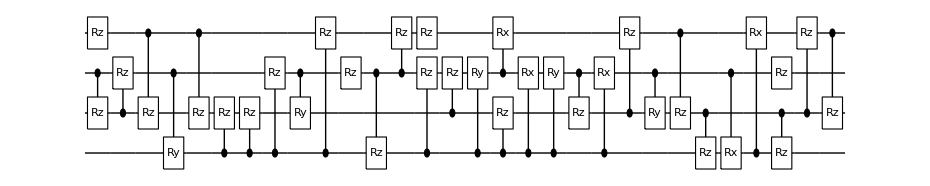

cost=8.65064×10^-8; ngates=34

runtime= 1.61554 minutes

cost=8.65064×10^-8 ;dist=0.000348291; globalphase=1.05477

Cycle1, @Sat 19 Mar 2022 22:52:01, fev:491, <E>: 0.05924739837476389 nansatz:8 merged-smallθ,metric,bf,gmerged: {1, 40, 0, 1, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:52:09, fev:598, <E>: 0.05924739837476389 nansatz:8 merged-smallθ,metric,bf,gmerged: {1, 40, 0, 1, 4}

Cycle3, @Sat 19 Mar 2022 22:52:26, fev:1046, <E>: 0.0031835710984666754 nansatz:13 merged-smallθ,metric,bf,gmerged: {1, 76, 7, 1, 5}

{{C_3[Rz_2[θ_101]],Rz_0[θ_99],C_3[Ry_1[θ_90]],C_3[Rz_0[θ_98]],C_2[Rx_3[θ_8]],C_0[Rz_3[θ_120]],C_2[Ry_0[θ_66]],C_0[Ry_2[θ_121]],C_1[Ry_2[θ_60]],C_0[Ry_2[θ_137]],Rz_1[θ_36],C_3[Rz_2[θ_84]],Rz_2[θ_136],C_1[Ry_2[θ_123]],C_2[Rx_3[θ_70]],C_0[Rz_1[θ_112]],C_2[Ry_0[θ_82]],C_3[Rx_1[θ_58]]},<|θ_8→3.14159,θ_36→-4.66374,θ_58→-3.14159,θ_60→-1.05141,θ_66→-3.14159,θ_70→-3.14159,θ_82→3.14159,θ_84→-1.24582,θ_90→3.14159,θ_98→3.22212,θ_99→-2.61207,θ_101→2.30062,θ_112→3.68888,θ_120→-1.01149,θ_121→0.440405,θ_123→0.335784,θ_136→0.0313014,θ_137→-0.174957|>,{2},2370,4,{merged, θsmall, metric, bruteforce}=,{1,119,7,1},Circuit within target precision is found}

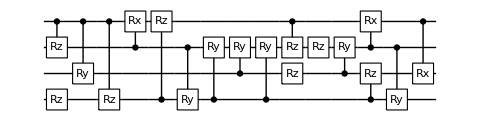

cost=1.24223×10^-8; ngates=18

runtime= 1.73579 minutes

cost=1.24223×10^-8 ;dist=0.000166025; globalphase=0.974538

Cycle1, @Sat 19 Mar 2022 22:53:55, fev:534, <E>: 0.033236859124485374 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 32, 4, 0, 3}

{{C_1[Rx_3[θ_81]],C_0[Rz_2[θ_4]],C_1[Rz_0[θ_80]],C_1[Rx_2[θ_50]],C_2[Rz_1[θ_31]],C_1[Rx_0[θ_66]],C_3[Rx_1[θ_75]],C_3[Rz_2[θ_64]],C_0[Rx_1[θ_40]],Rz_2[θ_74],C_2[Rx_1[θ_7]],C_1[Rx_0[θ_68]],C_2[Rz_1[θ_34]],C_1[Rx_3[θ_18]],C_1[Rx_2[θ_45]],C_3[Rz_0[θ_25]],Rz_2[θ_33]},<|θ_4→-0.976539,θ_7→0.58774,θ_18→-3.14163,θ_25→0.873824,θ_31→-4.76382,θ_33→-1.13357,θ_34→1.52028,θ_40→-0.587742,θ_45→3.14159,θ_50→-3.14159,θ_64→3.95548,θ_66→-3.14165,θ_68→3.14165,θ_74→-1.41494,θ_75→-0.137174,θ_80→-4.11731,θ_81→3.14162|>,{},1167,2,{merged, θsmall, metric, bruteforce}=,{1,62,10,0},Circuit within target precision is found}

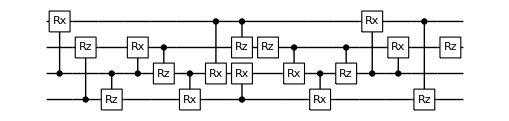

cost=7.81246×10^-9; ngates=17

runtime= 0.658004 minutes

cost=7.81246×10^-9 ;dist=0.000143172; globalphase=0.920777

Cycle1, @Sat 19 Mar 2022 22:54:33, fev:470, <E>: 1.35706893500398e-8 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 32, 0, 0, 1}

{{C_3[Ry_2[θ_1]],C_0[Rx_1[θ_3]],C_3[Rx_0[θ_5]],C_2[Rz_3[θ_7]],C_3[Rx_0[θ_10]],C_3[Rz_1[θ_11]],Ry_3[θ_16],C_3[Rz_2[θ_17]],C_0[Rz_3[θ_20]],C_2[Rx_3[θ_21]],C_3[Ry_0[θ_22]],C_0[Rx_1[θ_25]],C_3[Rz_1[θ_26]],C_1[Rz_0[θ_27]],C_2[Rz_3[θ_31]],C_3[Rz_2[θ_37]],C_3[Rx_2[θ_38]],Rz_2[θ_39]},<|θ_1→3.14159,θ_3→-3.14159,θ_5→-1.1547,θ_7→0.951687,θ_10→-1.98689,θ_11→-0.101834,θ_16→-0.450545,θ_17→-0.663393,θ_20→1.90249,θ_21→-0.450546,θ_22→-3.14159,θ_25→3.14159,θ_26→-3.86609,θ_27→1.07744,θ_31→-3.57757,θ_37→8.03561,θ_38→3.14159,θ_39→0.440151|>,{},611,1,{merged, θsmall, metric, bruteforce}=,{0,32,0,0},Circuit within target precision is found}

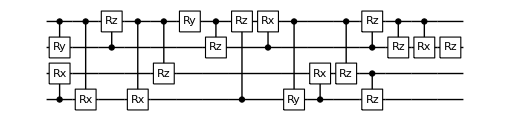

cost=1.35707×10^-8; ngates=18

runtime= 0.338647 minutes

cost=1.35707×10^-8 ;dist=0.000185104; globalphase=1.64313

Cycle1, @Sat 19 Mar 2022 22:54:51, fev:378, <E>: 0.05924741169160308 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 33, 8, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:54:59, fev:466, <E>: 0.05924741169160308 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 33, 8, 0, 1}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:55:16, fev:580, <E>: 0.05924741169160308 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 33, 8, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0592474

{{C_2[Rz_1[θ_29]],C_0[Rz_1[θ_25]],C_2[Rz_3[θ_30]],C_3[Rz_2[θ_24]],C_1[Rz_0[θ_9]],C_0[Rz_2[θ_15]],C_2[Rz_0[θ_13]],C_1[Rz_2[θ_39]],C_3[Rz_0[θ_36]]},<|θ_9→0.0836528,θ_13→-0.317147,θ_15→1.43809,θ_24→-0.658062,θ_25→-0.338127,θ_29→-0.0580687,θ_30→2.84739,θ_36→-0.163419,θ_39→2.06666|>,{2,3},638,3,{merged, θsmall, metric, bruteforce}=,{0,33,8,0},Compilation is either converging or stuck. }

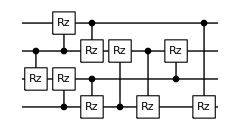

cost=0.0592474; ngates=9

runtime= 0.669455 minutes

cost=0.0592474 ;dist=0.360441; globalphase=0.39647

Cycle1, @Sat 19 Mar 2022 22:55:50, fev:576, <E>: 0.0592473629363065 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 39, 0, 0, 5}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:56:01, fev:661, <E>: 0.0592473629363065 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 39, 0, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:56:18, fev:772, <E>: 0.0592473629363065 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 39, 0, 0, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0592474

{{C_3[Rz_2[θ_9]],C_3[Ry_1[θ_41]],C_3[Rz_2[θ_12]],C_3[Ry_1[θ_47]],C_3[Rz_1[θ_26]],C_0[Rz_1[θ_18]],C_3[Rz_0[θ_22]],C_3[Rz_1[θ_19]],C_1[Rz_0[θ_43]],C_2[Rz_1[θ_35]],Rz_1[θ_32]},<|θ_9→-0.530316,θ_12→0.530913,θ_18→4.06583,θ_19→1.01081,θ_22→-2.04382,θ_26→7.32427,θ_32→-7.09055,θ_35→4.82037,θ_41→3.14159,θ_43→-1.19973,θ_47→3.14159|>,{2,3},858,3,{merged, θsmall, metric, bruteforce}=,{0,39,0,0},Compilation is either converging or stuck. }

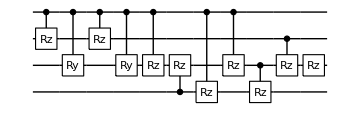

cost=0.0592474; ngates=11

runtime= 1.024 minutes

cost=0.0592474 ;dist=0.360441; globalphase=0.163615

```mathematica
Table[
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{10}];
,{t,times2}];
```

### Full compilation: {0.005,0.01,0.5,2}

```mathematica
resfullH2<<resfullH2.mx
```

Null resfullH2

```mathematica
conf=DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→50,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→0.001,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

Cycle1, @Sat 19 Mar 2022 22:56:45, fev:363, <E>: 2.9585460525893836e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 34, 3, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:56:59, fev:461, <E>: 2.9585460525893836e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 34, 3, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:57:16, fev:559, <E>: 2.9585460525893836e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 34, 3, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.95855×10^-7

{{C_1[Rz_2[θ_2]],Rz_3[θ_3],C_2[Rx_3[θ_5]],Rz_1[θ_14],C_0[Rz_2[θ_10]],C_2[Ry_3[θ_20]],C_1[Rz_3[θ_23]],C_2[Rz_1[θ_28]],C_3[Rz_0[θ_29]],C_0[Rz_1[θ_38]],C_0[Rz_3[θ_40]],Rz_0[θ_50],C_2[Ry_3[θ_47]]},<|θ_2→0.00205643,θ_3→0.107801,θ_5→-0.023593,θ_10→0.00241255,θ_14→-0.00403211,θ_20→0.222574,θ_23→0.00237477,θ_28→0.00126265,θ_29→0.21984,θ_38→0.00337379,θ_40→-0.216566,θ_47→-0.224057,θ_50→-0.111634|>,{2,3},607,3,{merged, θsmall, metric, bruteforce}=,{0,34,3,0},Compilation is either converging or stuck. }

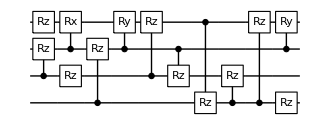

cost=2.95855×10^-7; ngates=13

runtime= 0.962267 minutes

cost=2.95855×10^-7 ;dist=0.00113668; globalphase=0.000476444

Cycle1, @Sat 19 Mar 2022 22:57:47, fev:449, <E>: 2.933275253802492e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 27, 6, 1, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 22:58:00, fev:544, <E>: 2.933275253802492e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 27, 6, 1, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:58:18, fev:646, <E>: 2.933275253802492e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 27, 6, 1, 5}

pruning exceeds the maxcost: 1.×10^-7; cost=2.93328×10^-7

{{Rz_2[θ_1],C_2[Rz_3[θ_2]],C_3[Rz_2[θ_4]],C_2[Rz_0[θ_10]],C_0[Rx_2[θ_11]],C_2[Rz_0[θ_13]],C_1[Rz_2[θ_19]],C_0[Rx_1[θ_21]],C_0[Rz_3[θ_24]],C_0[Ry_2[θ_25]],C_1[Rz_0[θ_27]],C_0[Rx_2[θ_29]],C_0[Rx_1[θ_36]],C_3[Rz_1[θ_37]],C_0[Ry_1[θ_38]],C_1[Rz_0[θ_45]]},<|θ_1→-0.00822561,θ_2→0.00109826,θ_4→0.00235592,θ_10→-2.56033,θ_11→0.332581,θ_13→2.5477,θ_19→0.00323142,θ_21→-0.165069,θ_24→0.00332822,θ_25→-0.319152,θ_27→1.09998,θ_29→-0.0951748,θ_36→0.141014,θ_37→0.00212562,θ_38→0.0859788,θ_45→-1.09105|>,{2,3},733,3,{merged, θsmall, metric, bruteforce}=,{0,27,6,1},Compilation is either converging or stuck. }

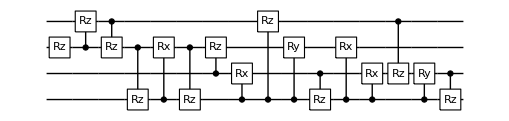

cost=2.93328×10^-7; ngates=16

runtime= 1.03138 minutes

cost=2.93328×10^-7 ;dist=0.0010656; globalphase=0.000482097

Cycle1, @Sat 19 Mar 2022 22:58:39, fev:332, <E>: 3.337716133477997e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 28, 6, 0, 2}

Cycle2, @Sat 19 Mar 2022 22:59:14, fev:808, <E>: 2.0569563541350533e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 58, 11, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Sat 19 Mar 2022 22:59:27, fev:890, <E>: 2.0569563541350533e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 58, 11, 0, 7}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Sat 19 Mar 2022 22:59:42, fev:986, <E>: 2.0569563541350533e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 58, 11, 0, 11}

pruning exceeds the maxcost: 1.×10^-7; cost=2.05696×10^-7

{{C_2[Rz_3[θ_56]],C_0[Rz_1[θ_59]],Rz_2[θ_57],Rz_3[θ_75],C_1[Ry_2[θ_61]],C_1[Rz_0[θ_64]],C_0[Rz_1[θ_67]],C_1[Ry_2[θ_69]],Rz_2[θ_72],C_0[Rz_1[θ_87]],C_3[Rz_2[θ_79]],C_2[Rz_3[θ_81]],C_1[Rz_3[θ_19]],Rz_2[θ_20],Rz_1[θ_8],C_2[Rz_0[θ_21]],C_2[Rz_1[θ_31]],C_3[Rz_2[θ_2]],Rz_2[θ_18],C_0[Rz_3[θ_1]],C_1[Rz_0[θ_48]]},<|θ_1→0.00335939,θ_2→-1.12959,θ_8→-0.00790805,θ_18→0.66036,θ_19→0.00242314,θ_20→-0.189237,θ_21→0.00235655,θ_31→0.0033058,θ_48→0.248548,θ_56→0.281222,θ_57→-0.0529688,θ_59→0.563555,θ_61→-0.00619452,θ_64→-0.2543,θ_67→-0.691325,θ_69→0.00619448,θ_72→0.00190845,θ_75→-0.420238,θ_79→0.293936,θ_81→0.557929,θ_87→0.136866|>,{3,4},1054,4,{merged, θsmall, metric, bruteforce}=,{0,58,11,0},I keep failing to lower the energy. }

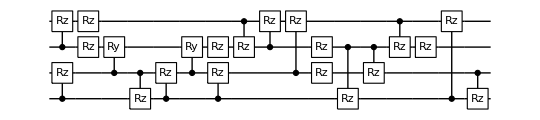

cost=2.05696×10^-7; ngates=21

runtime= 1.35335 minutes

cost=2.05696×10^-7 ;dist=0.000919318; globalphase=0.000496606

Cycle1, @Sat 19 Mar 2022 23:00:08, fev:349, <E>: 3.200512418422008e-7 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 26, 4, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:00:25, fev:451, <E>: 3.200512418422008e-7 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 26, 4, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:00:44, fev:551, <E>: 3.200512418422008e-7 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 26, 4, 0, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=3.20051×10^-7

{{Rz_1[θ_7],C_2[Rz_3[θ_3]],Ry_3[θ_5],C_2[Rz_1[θ_16]],C_3[Ry_0[θ_6]],C_3[Rx_0[θ_8]],C_3[Ry_0[θ_14]],C_3[Rx_0[θ_15]],C_2[Rz_3[θ_20]],C_2[Ry_0[θ_24]],C_3[Rz_1[θ_29]],C_0[Rz_2[θ_30]],Rx_3[θ_33],C_2[Rz_0[θ_41]],Rz_3[θ_40],Rz_2[θ_42],Rx_3[θ_44],C_2[Ry_0[θ_48]],Rx_0[θ_49],C_0[Rz_1[θ_50]]},<|θ_3→0.367603,θ_5→0.000275813,θ_6→-3.14339,θ_7→-0.00626655,θ_8→1.01348,θ_14→3.14499,θ_15→1.01346,θ_16→0.00331856,θ_20→-0.364104,θ_24→0.632717,θ_29→0.00241251,θ_30→0.00870961,θ_33→-0.522698,θ_40→0.000553129,θ_41→-0.00630868,θ_42→-0.0021208,θ_44→0.522649,θ_48→-0.63273,θ_49→-0.00064277,θ_50→0.00337378|>,{2,3},614,3,{merged, θsmall, metric, bruteforce}=,{0,26,4,0},Compilation is either converging or stuck. }

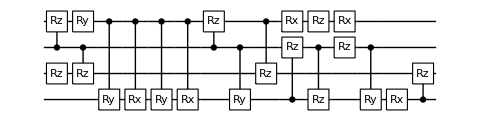

cost=3.20051×10^-7; ngates=20

runtime= 1.0332 minutes

cost=3.20051×10^-7 ;dist=0.00109538; globalphase=0.000402723

Cycle1, @Sat 19 Mar 2022 23:01:14, fev:279, <E>: 3.244583951511615e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {1, 26, 7, 0, 4}

Cycle2, @Sat 19 Mar 2022 23:01:52, fev:728, <E>: 2.217535405302229e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {1, 55, 13, 0, 8}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:02:11, fev:846, <E>: 2.217535405302229e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {1, 55, 13, 0, 14}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Sat 19 Mar 2022 23:02:26, fev:943, <E>: 2.217535405302229e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {1, 55, 13, 0, 18}

I'm slowing down. Number of gates is increased to 70 @cycle 5

Cycle5, @Sat 19 Mar 2022 23:02:49, fev:1054, <E>: 2.217535405302229e-7 nansatz:21 merged-smallθ,metric,bf,gmerged: {1, 55, 13, 0, 20}

pruning exceeds the maxcost: 1.×10^-7; cost=2.21754×10^-7

{{C_0[Rz_1[θ_4]],C_1[Rz_2[θ_5]],Rz_0[θ_24],C_2[Rz_1[θ_6]],C_2[Ry_3[θ_11]],C_1[Rz_3[θ_15]],Rz_2[θ_21],Ry_1[θ_51],C_2[Rz_0[θ_28]],C_3[Rz_2[θ_29]],Rx_3[θ_31],C_2[Rz_3[θ_44]],Rx_3[θ_45],C_3[Rx_1[θ_55]],Ry_1[θ_56],C_0[Rz_3[θ_61]],C_0[Rz_2[θ_64]],Rz_3[θ_72],C_3[Ry_1[θ_79]],C_3[Rz_0[θ_82]],C_3[Rx_1[θ_88]]},<|θ_4→0.00337501,θ_5→0.0136865,θ_6→-0.0103806,θ_11→-0.239541,θ_15→-0.00117054,θ_21→-0.0832023,θ_24→0.0985878,θ_28→-0.392021,θ_29→-0.237008,θ_31→0.786842,θ_44→0.339094,θ_45→-0.786855,θ_51→0.00950965,θ_55→0.360958,θ_56→-0.00948679,θ_61→-0.188035,θ_64→0.394433,θ_72→-0.023392,θ_79→-0.000631345,θ_82→0.191418,θ_88→-0.360935|>,{3,4,5},1134,5,{merged, θsmall, metric, bruteforce}=,{1,55,13,0},I keep failing to lower the energy. }

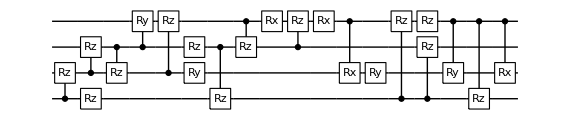

cost=2.21754×10^-7; ngates=21

runtime= 1.95848 minutes

cost=2.21754×10^-7 ;dist=0.000933112; globalphase=0.000487616

Cycle1, @Sat 19 Mar 2022 23:03:11, fev:357, <E>: 3.315617769228396e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 25, 0, 0, 6}

Cycle2, @Sat 19 Mar 2022 23:04:01, fev:853, <E>: 2.1100916747229803e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 56, 0, 0, 7}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:04:20, fev:969, <E>: 2.1100916747229803e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 56, 0, 0, 10}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Sat 19 Mar 2022 23:04:41, fev:1067, <E>: 2.1100916747229803e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 56, 0, 0, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=2.11009×10^-7

{{Rz_0[θ_7],C_3[Ry_0[θ_29]],C_3[Rx_0[θ_54]],C_2[Ry_0[θ_30]],C_1[Rz_3[θ_61]],C_2[Rx_1[θ_52]],C_3[Ry_0[θ_86]],C_1[Rz_2[θ_67]],Rz_2[θ_83],C_2[Ry_0[θ_66]],C_2[Ry_0[θ_44]],Rz_0[θ_22],C_2[Ry_1[θ_59]],C_3[Rz_1[θ_3]],C_2[Rx_1[θ_68]],C_3[Rz_1[θ_46]],C_2[Rz_3[θ_84]],Rz_1[θ_85],C_3[Ry_0[θ_5]],C_3[Rx_0[θ_49]],C_3[Rz_0[θ_13]],Rz_0[θ_60],C_3[Rz_2[θ_57]],C_1[Rz_2[θ_10]],C_1[Rz_0[θ_21]],C_3[Rx_0[θ_72]],C_3[Rz_2[θ_78]],C_3[Rx_0[θ_55]],C_2[Rz_0[θ_32]],C_3[Rz_1[θ_71]],C_2[Ry_1[θ_58]],C_3[Rz_2[θ_34]],C_0[Rz_3[θ_43]]},<|θ_3→-0.0150353,θ_5→-1.47235,θ_7→0.927386,θ_10→0.031943,θ_13→-0.821827,θ_21→0.00337168,θ_22→-1.20918,θ_29→1.04549,θ_30→-1.04208,θ_32→0.00241078,θ_34→-0.488245,θ_43→0.0722478,θ_44→0.848019,θ_46→-0.186706,θ_49→-0.971321,θ_52→0.00203828,θ_54→-0.417338,θ_55→0.0656171,θ_57→0.46439,θ_58→-0.00155735,θ_59→0.00153493,θ_60→0.311656,θ_61→-0.221157,θ_66→0.19406,θ_67→-0.0286372,θ_68→-0.0020131,θ_71→0.425329,θ_72→-0.10269,θ_78→-0.126047,θ_83→0.0755352,θ_84→0.153379,θ_85→-0.113518,θ_86→0.451756|>,{3,4},1179,4,{merged, θsmall, metric, bruteforce}=,{0,56,0,0},Compilation is either converging or stuck. }

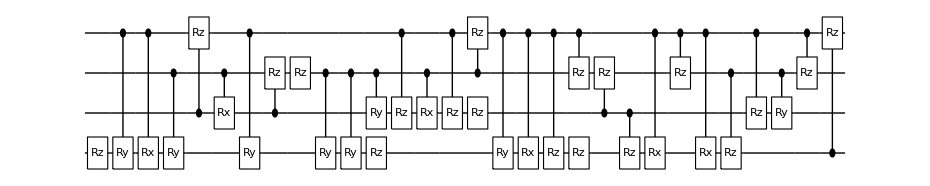

cost=2.11009×10^-7; ngates=33

runtime= 1.84736 minutes

cost=2.11009×10^-7 ;dist=0.000913236; globalphase=0.000481101

Cycle1, @Sat 19 Mar 2022 23:05:09, fev:301, <E>: 2.348499510418378e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 19, 8, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:05:26, fev:405, <E>: 2.348499510418378e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 19, 8, 0, 1}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:05:45, fev:527, <E>: 2.348499510418378e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 19, 8, 0, 3}

pruning exceeds the maxcost: 1.×10^-7; cost=2.3485×10^-7

{{C_2[Rz_0[θ_14]],C_0[Ry_2[θ_1]],C_0[Rz_1[θ_19]],C_3[Rz_2[θ_7]],C_2[Rz_1[θ_6]],C_0[Ry_1[θ_18]],C_3[Rx_1[θ_8]],C_0[Ry_2[θ_28]],Rz_2[θ_2],C_0[Rx_1[θ_46]],C_0[Rz_2[θ_5]],C_0[Ry_1[θ_20]],C_0[Rx_2[θ_26]],C_3[Rz_1[θ_22]],C_0[Rx_2[θ_13]],C_1[Rz_3[θ_48]],C_0[Ry_2[θ_34]],C_0[Rz_1[θ_35]],C_3[Rx_1[θ_38]],C_0[Rz_1[θ_4]],C_0[Rz_3[θ_30]],C_0[Rx_1[θ_16]],C_2[Rz_3[θ_32]]},<|θ_1→-0.00191911,θ_2→-0.00837462,θ_4→-0.0195708,θ_5→0.00584065,θ_6→0.00330656,θ_7→0.0153777,θ_8→0.033748,θ_13→-0.163804,θ_14→-0.00342809,θ_16→0.212008,θ_18→-0.0344859,θ_19→0.00661592,θ_20→0.0320924,θ_22→-0.00998816,θ_26→0.163841,θ_28→-0.0185358,θ_30→0.00331678,θ_32→-0.0118904,θ_34→0.0204548,θ_35→0.00974698,θ_38→-0.0338325,θ_46→-0.212127,θ_48→0.0130441|>,{2,3},611,3,{merged, θsmall, metric, bruteforce}=,{0,19,8,0},Compilation is either converging or stuck. }

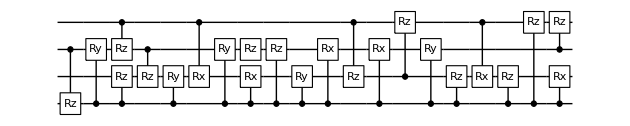

cost=2.3485×10^-7; ngates=23

runtime= 0.960982 minutes

cost=2.3485×10^-7 ;dist=0.000938098; globalphase=0.000463068

Cycle1, @Sat 19 Mar 2022 23:06:18, fev:348, <E>: 2.525575686362913e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {1, 31, 0, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:06:34, fev:456, <E>: 2.525575686362913e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {1, 31, 0, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:06:48, fev:553, <E>: 2.525575686362913e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {1, 31, 0, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.52558×10^-7

{{C_2[Ry_0[θ_1]],C_1[Rz_3[θ_2]],C_3[Rz_2[θ_3]],Rz_0[θ_29],C_2[Ry_1[θ_6]],C_3[Ry_1[θ_9]],C_1[Rz_2[θ_13]],C_2[Rz_1[θ_19]],C_3[Ry_1[θ_22]],C_1[Rz_2[θ_23]],Rz_2[θ_25],C_3[Rz_1[θ_35]],C_2[Rx_0[θ_39]],C_2[Ry_1[θ_41]],C_0[Rz_3[θ_43]],C_2[Ry_0[θ_45]],Rz_0[θ_47],C_1[Rz_0[θ_48]]},<|θ_1→0.114941,θ_2→0.0009618,θ_3→0.00348851,θ_6→-0.348811,θ_9→-0.205956,θ_13→0.00343773,θ_19→-0.00420779,θ_22→0.20597,θ_23→0.00448427,θ_25→-0.00347108,θ_29→0.404407,θ_35→0.00115999,θ_39→0.0453959,θ_41→0.348822,θ_43→0.00330686,θ_45→-0.105633,θ_47→-0.409008,θ_48→0.00337376|>,{2,3},599,3,{merged, θsmall, metric, bruteforce}=,{1,31,0,0},Compilation is either converging or stuck. }

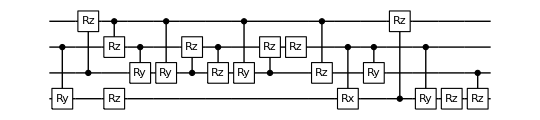

cost=2.52558×10^-7; ngates=18

runtime= 0.938451 minutes

cost=2.52558×10^-7 ;dist=0.00104729; globalphase=0.0005386

Cycle1, @Sat 19 Mar 2022 23:07:06, fev:264, <E>: 3.3742099059264063e-7 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 30, 7, 0, 3}

Cycle2, @Sat 19 Mar 2022 23:07:31, fev:768, <E>: 2.0994754168501828e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {2, 57, 7, 0, 6}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:07:45, fev:864, <E>: 2.0994754168501828e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {2, 57, 7, 0, 7}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Sat 19 Mar 2022 23:08:06, fev:960, <E>: 2.0994754168501828e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {2, 57, 7, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=2.09948×10^-7

{{C_3[Rz_2[θ_1]],C_1[Rz_2[θ_2]],C_1[Rz_3[θ_5]],C_3[Ry_0[θ_6]],Rz_1[θ_30],C_3[Ry_0[θ_31]],C_2[Rz_0[θ_35]],Rz_2[θ_40],C_0[Rx_2[θ_53]],C_0[Rz_2[θ_54]],Rz_2[θ_58],C_3[Rz_0[θ_60]],C_0[Rx_2[θ_63]],C_3[Rz_0[θ_64]],C_0[Rx_1[θ_66]],C_0[Ry_2[θ_70]],C_3[Rz_2[θ_71]],C_2[Rz_0[θ_72]],C_0[Rz_3[θ_75]],C_0[Rz_1[θ_83]],C_0[Rz_3[θ_84]],C_0[Rz_2[θ_85]],C_0[Rz_3[θ_88]],C_0[Rx_1[θ_89]]},<|θ_1→-0.000504649,θ_2→0.00332095,θ_5→0.00244261,θ_6→-0.000890491,θ_30→-0.00334227,θ_31→0.000890491,θ_35→-0.162982,θ_40→-0.915982,θ_53→-0.585651,θ_54→-0.708773,θ_58→0.911157,θ_60→-0.0275289,θ_63→0.576192,θ_64→0.0288817,θ_66→-0.0487422,θ_70→0.111335,θ_71→0.0039953,θ_72→0.158107,θ_75→0.499433,θ_83→0.00326348,θ_84→-0.0626404,θ_85→0.749102,θ_88→-0.434796,θ_89→0.0487424|>,{3,4},1041,4,{merged, θsmall, metric, bruteforce}=,{2,57,7,0},I keep failing to lower the energy. }

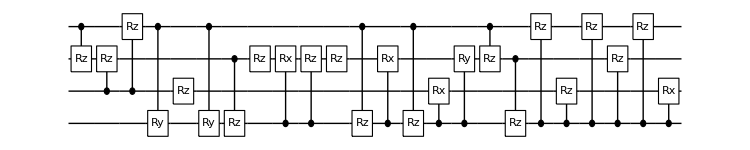

cost=2.09948×10^-7; ngates=24

runtime= 1.26404 minutes

cost=2.09948×10^-7 ;dist=0.000945675; globalphase=0.000473571

Cycle1, @Sat 19 Mar 2022 23:08:30, fev:196, <E>: 2.530328723215902e-7 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 20, 8, 0, 6}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:08:49, fev:319, <E>: 2.530328723215902e-7 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 20, 8, 0, 9}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:09:10, fev:427, <E>: 2.530328723215902e-7 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 20, 8, 0, 11}

pruning exceeds the maxcost: 1.×10^-7; cost=2.53033×10^-7

{{C_1[Ry_2[θ_4]],C_1[Rx_2[θ_18]],C_2[Rz_3[θ_7]],C_1[Rz_2[θ_41]],Rz_3[θ_17],C_0[Rx_1[θ_29]],Rz_2[θ_38],C_3[Rz_1[θ_1]],C_0[Rx_1[θ_24]],C_1[Rx_2[θ_9]],C_0[Rz_2[θ_15]],C_3[Ry_0[θ_28]],C_1[Rz_0[θ_21]],C_1[Rx_2[θ_23]],C_0[Rz_3[θ_39]],C_1[Ry_2[θ_45]],C_2[Rz_0[θ_19]],C_2[Rz_1[θ_16]],C_3[Ry_0[θ_22]],Rz_0[θ_48]},<|θ_1→0.00240923,θ_4→-0.00261788,θ_7→0.00406724,θ_9→-0.343325,θ_15→0.00147641,θ_16→-0.00583418,θ_17→-0.00146343,θ_18→0.0501777,θ_19→0.000939738,θ_21→0.00336974,θ_22→0.00157479,θ_23→0.293132,θ_24→-0.0222449,θ_28→-0.00157478,θ_29→0.0222453,θ_38→-0.00279783,θ_39→0.00332486,θ_41→0.00917775,θ_45→0.00243134,θ_48→-0.00386995|>,{2,3},470,3,{merged, θsmall, metric, bruteforce}=,{0,20,8,0},Compilation is either converging or stuck. }

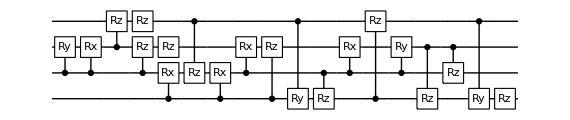

cost=2.53033×10^-7; ngates=20

runtime= 0.954266 minutes

cost=2.53033×10^-7 ;dist=0.00106968; globalphase=0.00049908

Cycle1, @Sat 19 Mar 2022 23:09:54, fev:524, <E>: 0.000020594544103746948 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 24, 8, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:10:14, fev:666, <E>: 0.000020594544103746948 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 24, 8, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:10:40, fev:823, <E>: 0.000020594544103746948 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 24, 8, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205945

{{Rz_3[θ_1],C_1[Rz_0[θ_3]],C_2[Ry_0[θ_8]],C_1[Rz_2[θ_10]],C_2[Ry_0[θ_11]],C_3[Rz_2[θ_13]],C_0[Rz_1[θ_19]],C_3[Rz_0[θ_22]],C_0[Rx_1[θ_26]],Rz_0[θ_28],Ry_1[θ_33],C_0[Rx_1[θ_34]],Ry_0[θ_41],C_2[Rz_1[θ_36]],Ry_1[θ_42],C_2[Rz_0[θ_46]],C_3[Rz_1[θ_43]],Ry_0[θ_47]},<|θ_1→0.0227117,θ_3→0.116142,θ_8→0.0156958,θ_10→0.00986516,θ_11→-0.0157055,θ_13→0.0348515,θ_19→-0.0833886,θ_22→0.0331836,θ_26→0.0715474,θ_28→-0.103865,θ_33→-0.0136223,θ_34→-0.0717142,θ_36→0.0232967,θ_41→-0.002752,θ_42→0.0136075,θ_43→0.0248486,θ_46→0.0241227,θ_47→0.00275681|>,{2,3},889,3,{merged, θsmall, metric, bruteforce}=,{0,24,8,0},Compilation is either converging or stuck. }

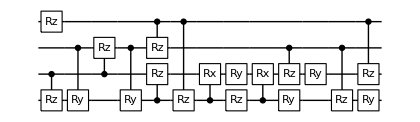

cost=0.0000205945; ngates=18

runtime= 1.41896 minutes

cost=0.0000205945 ;dist=0.00906577; globalphase=0.00467414

Cycle1, @Sat 19 Mar 2022 23:11:20, fev:518, <E>: 0.000020631374341606445 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 26, 7, 3, 2}

Cycle2, @Sat 19 Mar 2022 23:12:17, fev:1291, <E>: 0.000020529405330482753 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 54, 7, 4, 5}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:12:40, fev:1431, <E>: 0.000020529405330482753 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 54, 7, 4, 7}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Sat 19 Mar 2022 23:12:59, fev:1549, <E>: 0.000020529405330482753 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 54, 7, 4, 9}

I'm slowing down. Number of gates is increased to 70 @cycle 5

Cycle5, @Sat 19 Mar 2022 23:13:27, fev:1685, <E>: 0.000020529405330482753 nansatz:24 merged-smallθ,metric,bf,gmerged: {1, 54, 7, 4, 17}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205294

{{C_2[Ry_1[θ_52]],Rx_1[θ_56],Rz_2[θ_59],C_0[Rz_2[θ_68]],Rz_1[θ_58],C_3[Rz_0[θ_71]],Rx_1[θ_73],C_2[Ry_1[θ_75]],Rz_0[θ_77],C_0[Rz_2[θ_80]],Rx_1[θ_84],Rz_2[θ_86],C_2[Rx_1[θ_88]],C_1[Rz_0[θ_89]],Rz_0[θ_9],C_3[Rz_1[θ_8]],C_3[Ry_2[θ_17]],C_0[Ry_2[θ_21]],C_0[Ry_2[θ_24]],C_1[Rz_0[θ_35]],C_3[Ry_2[θ_34]],C_2[Rz_3[θ_37]],C_2[Rz_0[θ_42]],C_0[Rz_3[θ_44]]},<|θ_8→0.0240934,θ_9→1.2401,θ_17→2.77535,θ_21→-0.00660285,θ_24→0.00660285,θ_34→-2.77535,θ_35→-0.731078,θ_37→0.0348825,θ_42→0.0327951,θ_44→0.00977856,θ_52→1.28099,θ_56→0.00100328,θ_58→-0.0457794,θ_59→0.346664,θ_68→-0.835068,θ_71→0.023407,θ_73→-0.000172031,θ_75→-1.28068,θ_77→-1.30221,θ_80→0.826398,θ_84→-0.000846609,θ_86→-0.319985,θ_88→-0.0432597,θ_89→0.764816|>,{3,4,5},1794,5,{merged, θsmall, metric, bruteforce}=,{1,54,7,4},I keep failing to lower the energy. }

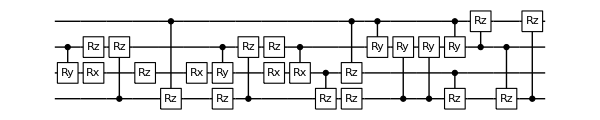

cost=0.0000205294; ngates=24

runtime= 2.84974 minutes

cost=0.0000205294 ;dist=0.00913449; globalphase=0.00486239

Cycle1, @Sat 19 Mar 2022 23:14:27, fev:776, <E>: 0.000020556968955309785 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 32, 6, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:14:42, fev:888, <E>: 0.000020556968955309785 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 32, 6, 0, 0}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:14:59, fev:995, <E>: 0.000020556968955309785 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 32, 6, 0, 0}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000020557

{{C_2[Rz_0[θ_2]],C_2[Rz_1[θ_4]],Rz_2[θ_24],C_1[Rz_0[θ_7]],C_0[Ry_3[θ_12]],C_3[Rz_0[θ_15]],C_0[Rx_3[θ_19]],C_0[Ry_3[θ_26]],C_0[Rz_1[θ_32]],C_2[Rz_3[θ_36]],C_0[Rz_2[θ_42]],C_3[Rz_1[θ_38]]},<|θ_2→-0.183697,θ_4→0.033126,θ_7→0.125111,θ_12→-0.984268,θ_15→0.0243317,θ_19→-0.0180362,θ_24→-0.0815569,θ_26→0.98415,θ_32→-0.0914182,θ_36→0.0350501,θ_38→0.0240651,θ_42→0.207804|>,{2,3},1119,3,{merged, θsmall, metric, bruteforce}=,{0,32,6,0},Compilation is either converging or stuck. }

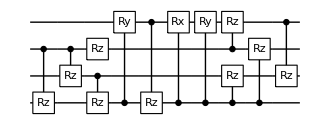

cost=0.000020557; ngates=12

runtime= 1.36974 minutes

cost=0.000020557 ;dist=0.00919793; globalphase=0.00487386

Cycle1, @Sat 19 Mar 2022 23:15:39, fev:448, <E>: 0.000020542081784258315 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 32, 8, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:15:51, fev:547, <E>: 0.000020542081784258315 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 32, 8, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:16:09, fev:666, <E>: 0.000020542081784258315 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 32, 8, 0, 2}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205421

{{C_2[Rz_1[θ_8]],C_1[Rz_0[θ_10]],C_1[Rz_3[θ_11]],C_3[Rz_2[θ_12]],C_3[Rz_0[θ_17]],C_0[Rz_2[θ_28]],Rz_3[θ_22],C_1[Rz_2[θ_35]],C_2[Rz_3[θ_36]],C_2[Rz_0[θ_43]]},<|θ_8→-0.0336729,θ_10→0.0337781,θ_11→0.0241236,θ_12→-0.14747,θ_17→0.0332259,θ_22→-0.0808854,θ_28→0.125446,θ_35→0.0667488,θ_36→0.182337,θ_43→-0.101318|>,{2,3},709,3,{merged, θsmall, metric, bruteforce}=,{0,32,8,0},Compilation is either converging or stuck. }

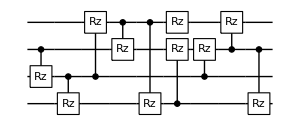

cost=0.0000205421; ngates=10

runtime= 1.03421 minutes

cost=0.0000205421 ;dist=0.00908392; globalphase=0.00485159

Cycle1, @Sat 19 Mar 2022 23:16:55, fev:627, <E>: 0.000020517705063949343 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:17:13, fev:744, <E>: 0.000020517705063949343 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:17:33, fev:883, <E>: 0.000020517705063949343 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205177

{{C_3[Rz_0[θ_3]],C_2[Rx_1[θ_8]],C_3[Rz_0[θ_7]],C_2[Rz_1[θ_11]],C_2[Rx_1[θ_12]],Rz_3[θ_25],C_0[Rz_2[θ_13]],C_2[Rz_1[θ_18]],C_2[Ry_1[θ_23]],C_2[Rz_3[θ_26]],C_2[Rx_1[θ_27]],C_1[Rz_2[θ_29]],C_3[Ry_1[θ_34]],C_2[Rz_0[θ_36]],C_3[Ry_1[θ_39]],C_3[Ry_1[θ_42]],C_1[Rz_0[θ_44]],C_1[Rz_3[θ_45]],C_0[Rz_3[θ_48]]},<|θ_3→0.277682,θ_7→-0.392608,θ_8→-0.455222,θ_11→0.658407,θ_12→0.461732,θ_13→-0.0227813,θ_18→-0.641198,θ_23→0.273169,θ_25→-0.0812165,θ_26→0.0348826,θ_27→0.0898771,θ_29→0.0674684,θ_34→-1.33591,θ_36→0.0469063,θ_39→-0.242524,θ_42→1.57844,θ_44→0.0337376,θ_45→0.024125,θ_48→0.148112|>,{2,3},965,3,{merged, θsmall, metric, bruteforce}=,{0,31,0,0},I keep failing to lower the energy. }

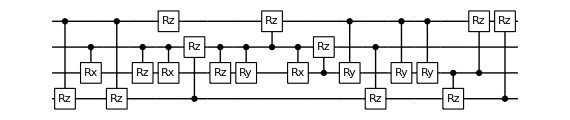

cost=0.0000205177; ngates=19

runtime= 1.38842 minutes

cost=0.0000205177 ;dist=0.00906049; globalphase=0.00485332

Cycle1, @Sat 19 Mar 2022 23:18:08, fev:452, <E>: 0.000020617254474775137 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 31, 5, 1, 5}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:18:20, fev:543, <E>: 0.000020617254474775137 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 31, 5, 1, 9}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:18:36, fev:646, <E>: 0.000020617254474775137 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 31, 5, 1, 12}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000206173

{{Rz_2[θ_21],C_3[Rz_0[θ_41]],C_2[Rz_1[θ_45]],C_0[Rz_3[θ_48]],Rz_1[θ_39],C_2[Rz_3[θ_7]],C_2[Rz_0[θ_49]],C_2[Rz_0[θ_26]],C_0[Rz_2[θ_6]],C_0[Rz_1[θ_27]],C_1[Rz_3[θ_46]],C_1[Rz_3[θ_29]]},<|θ_6→0.105615,θ_7→0.0348062,θ_21→-0.0304644,θ_26→-0.516223,θ_27→0.033738,θ_29→0.00858068,θ_39→-0.0506033,θ_41→0.0481252,θ_45→0.0331853,θ_46→0.0154672,θ_48→-0.0140897,θ_49→0.434738|>,{2,3},688,3,{merged, θsmall, metric, bruteforce}=,{0,31,5,1},Compilation is either converging or stuck. }

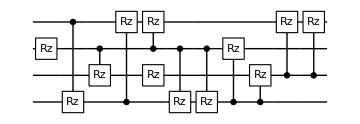

cost=0.0000206173; ngates=12

runtime= 1.01315 minutes

cost=0.0000206173 ;dist=0.00929374; globalphase=0.00487307

Cycle1, @Sat 19 Mar 2022 23:19:10, fev:463, <E>: 0.000020570627900728944 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 30, 7, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:19:19, fev:560, <E>: 0.000020570627900728944 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 30, 7, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:19:41, fev:702, <E>: 0.000020570627900728944 nansatz:12 merged-smallθ,metric,bf,gmerged: {1, 30, 7, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205706

{{C_1[Rz_2[θ_13]],C_0[Rz_3[θ_16]],C_1[Rx_2[θ_20]],Rz_3[θ_10],C_1[Rz_0[θ_23]],C_2[Rz_1[θ_31]],C_0[Rz_2[θ_8]],Rz_0[θ_18],C_1[Rx_2[θ_32]],Rz_2[θ_27],C_1[Rz_3[θ_6]],C_2[Rz_3[θ_2]]},<|θ_2→0.0348826,θ_6→0.024125,θ_8→0.0241618,θ_10→-0.0237532,θ_13→0.0675324,θ_16→0.0331856,θ_18→-0.0340103,θ_20→0.0431756,θ_23→0.0337378,θ_27→-0.0232802,θ_31→-0.0343124,θ_32→-0.0431775|>,{2,3},743,3,{merged, θsmall, metric, bruteforce}=,{1,30,7,0},Compilation is either converging or stuck. }

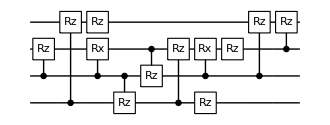

cost=0.0000205706; ngates=12

runtime= 0.979248 minutes

cost=0.0000205706 ;dist=0.00907422; globalphase=0.00485121

Cycle1, @Sat 19 Mar 2022 23:20:17, fev:438, <E>: 0.00002053111553224074 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 1, 7}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:20:35, fev:580, <E>: 0.00002053111553224074 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 1, 10}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:20:56, fev:731, <E>: 0.00002053111553224074 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 1, 11}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205311

{{C_1[Rz_3[θ_42]],C_2[Rz_0[θ_37]],Rz_1[θ_7],C_1[Rz_2[θ_17]],C_3[Rz_2[θ_26]],C_1[Ry_0[θ_32]],C_1[Rz_0[θ_28]],C_1[Ry_0[θ_44]],C_2[Rz_1[θ_36]],C_3[Rz_0[θ_33]],C_0[Rz_2[θ_6]],C_3[Rz_1[θ_47]]},<|θ_6→0.12557,θ_7→-0.0813948,θ_17→-0.116153,θ_26→0.0349374,θ_28→0.0337983,θ_32→0.0022852,θ_33→0.0332462,θ_36→0.149065,θ_37→-0.101387,θ_42→0.0446857,θ_44→-0.00228522,θ_47→-0.0205595|>,{2,3},785,3,{merged, θsmall, metric, bruteforce}=,{0,35,0,1},I keep failing to lower the energy. }

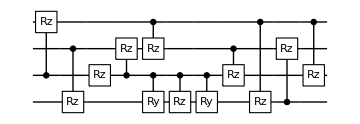

cost=0.0000205311; ngates=12

runtime= 1.15035 minutes

cost=0.0000205311 ;dist=0.00914175; globalphase=0.00483752

Cycle1, @Sat 19 Mar 2022 23:21:48, fev:566, <E>: 0.00002056467215305613 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 32, 5, 1, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:22:05, fev:700, <E>: 0.00002056467215305613 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 32, 5, 1, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:22:23, fev:822, <E>: 0.00002056467215305613 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 32, 5, 1, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205647

{{C_1[Rz_2[θ_12]],C_0[Rz_1[θ_13]],C_3[Rz_0[θ_17]],C_3[Rz_2[θ_18]],C_1[Rz_0[θ_22]],Rx_3[θ_21],C_2[Rz_1[θ_26]],C_2[Rz_0[θ_27]],C_1[Rz_3[θ_34]],Rz_2[θ_38],Rx_3[θ_43],C_2[Rz_3[θ_48]]},<|θ_12→0.193712,θ_13→0.12662,θ_17→0.0335099,θ_18→0.0144277,θ_21→0.00105434,θ_22→-0.0925648,θ_26→-0.160354,θ_27→0.0244493,θ_34→0.0241611,θ_38→-0.081744,θ_43→-0.00105434,θ_48→0.0204903|>,{2,3},863,3,{merged, θsmall, metric, bruteforce}=,{0,32,5,1},Compilation is either converging or stuck. }

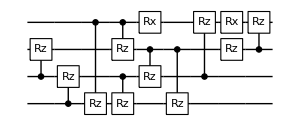

cost=0.0000205647; ngates=12

runtime= 1.37354 minutes

cost=0.0000205647 ;dist=0.00909693; globalphase=0.00476557

Cycle1, @Sat 19 Mar 2022 23:23:13, fev:743, <E>: 0.000020544338954708863 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 34, 0, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:23:26, fev:852, <E>: 0.000020544338954708863 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 34, 0, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:23:49, fev:989, <E>: 0.000020544338954708863 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 34, 0, 0, 5}

I'm slowing down. Number of gates is increased to 70 @cycle 4

Cycle4, @Sat 19 Mar 2022 23:24:12, fev:1129, <E>: 0.000020544338954708863 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 34, 0, 0, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205443

{{Rz_2[θ_1],C_3[Rz_0[θ_2]],C_1[Rz_3[θ_4]],C_0[Rz_3[θ_6]],C_2[Rx_0[θ_8]],C_0[Rz_2[θ_11]],C_2[Rz_3[θ_12]],C_1[Rz_2[θ_15]],C_2[Ry_0[θ_18]],C_2[Rz_1[θ_19]],C_0[Rz_2[θ_22]],C_2[Ry_0[θ_36]],C_1[Rx_0[θ_38]],C_2[Rx_0[θ_41]],C_1[Rx_0[θ_44]],C_1[Rz_0[θ_47]]},<|θ_1→-0.0809465,θ_2→0.0470111,θ_4→0.0240094,θ_6→-0.0138923,θ_8→1.46287,θ_11→-0.458959,θ_12→0.034767,θ_15→0.0672285,θ_18→0.783128,θ_19→-0.0341624,θ_22→0.597774,θ_36→-0.714325,θ_38→0.306026,θ_41→-1.25328,θ_44→-0.306026,θ_47→0.0336235|>,{2,3,4},1236,4,{merged, θsmall, metric, bruteforce}=,{0,34,0,0},Compilation is either converging or stuck. }

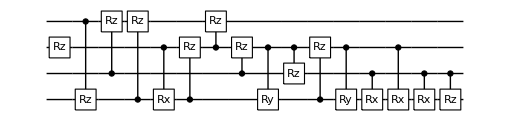

cost=0.0000205443; ngates=16

runtime= 1.79972 minutes

cost=0.0000205443 ;dist=0.0090717; globalphase=0.00491251

Cycle1, @Sat 19 Mar 2022 23:24:47, fev:488, <E>: 0.0019977140849997133 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 31, 6, 1, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:24:58, fev:576, <E>: 0.0019977140849997133 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 31, 6, 1, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:25:14, fev:671, <E>: 0.0019977140849997133 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 31, 6, 1, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.00199771

{{Ry_0[θ_2],Rx_0[θ_4],Ry_0[θ_6],C_0[Rz_3[θ_7]],C_1[Rz_3[θ_10]],C_2[Rz_1[θ_12]],Rz_3[θ_14],Rz_2[θ_23],C_1[Rz_0[θ_22]],C_2[Rz_3[θ_26]],C_3[Rz_1[θ_44]],C_0[Rz_2[θ_45]]},<|θ_2→-1.56954,θ_4→0.340434,θ_6→1.56961,θ_7→0.331724,θ_10→0.916467,θ_12→0.331862,θ_14→-0.574816,θ_22→0.337418,θ_23→0.103067,θ_26→0.348825,θ_44→-0.675214,θ_45→0.241252|>,{2,3},735,3,{merged, θsmall, metric, bruteforce}=,{0,31,6,1},Compilation is either converging or stuck. }

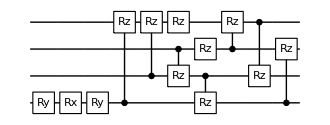

cost=0.00199771; ngates=12

runtime= 0.997365 minutes

cost=0.00199771 ;dist=0.0905747; globalphase=0.0484913

Cycle1, @Sat 19 Mar 2022 23:25:56, fev:540, <E>: 0.0019976917080879453 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 26, 9, 1, 6}

Cycle2, @Sat 19 Mar 2022 23:26:25, fev:953, <E>: 0.0015097067374398865 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 51, 19, 1, 9}

Cycle3, @Sat 19 Mar 2022 23:27:13, fev:1574, <E>: 0.0005304736110720576 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 80, 27, 1, 14}

Cycle4, @Sat 19 Mar 2022 23:28:18, fev:2641, <E>: 0.0005010223249357626 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 110, 35, 1, 18}

Cycle5, @Sat 19 Mar 2022 23:29:47, fev:3998, <E>: 0.00024870653440134394 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 145, 39, 1, 21}

Cycle6, @Sat 19 Mar 2022 23:31:25, fev:5304, <E>: 0.00024389044163275475 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 175, 47, 1, 25}

Cycle7, @Sat 19 Mar 2022 23:32:21, fev:6423, <E>: 0.00001720204508692813 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 204, 57, 1, 28}

Cycle8, @Sat 19 Mar 2022 23:33:35, fev:7302, <E>: 7.591712402055251e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 239, 62, 1, 29}

Cycle9, @Sat 19 Mar 2022 23:35:09, fev:8614, <E>: 2.491611238442104e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 270, 69, 1, 29}

I'm slowing down. Number of gates is increased to 48 @cycle 10

Cycle10, @Sat 19 Mar 2022 23:35:26, fev:8730, <E>: 2.491611238442104e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 270, 69, 1, 29}

{{C_0[Rz_1[θ_179]],C_2[Rz_3[θ_7]],C_0[Rx_2[θ_16]],Rz_0[θ_384],C_0[Rx_3[θ_44]],C_3[Rz_1[θ_391]],C_0[Ry_1[θ_76]],C_3[Rx_0[θ_390]],C_2[Ry_0[θ_349]],C_3[Rz_2[θ_23]],C_2[Rz_3[θ_331]],C_1[Rz_2[θ_292]],C_0[Rz_3[θ_405]],C_3[Ry_0[θ_401]],C_2[Rz_0[θ_125]],C_2[Rz_1[θ_351]],C_3[Rx_0[θ_403]],C_1[Rz_3[θ_357]],C_1[Rz_0[θ_9]],C_2[Rx_0[θ_348]],C_0[Rz_3[θ_114]],C_0[Rz_1[θ_380]],Rz_0[θ_319],C_2[Rx_0[θ_312]],C_0[Ry_1[θ_82]],C_3[Rz_1[θ_400]],C_0[Rx_2[θ_30]],Rz_0[θ_130],C_0[Rz_3[θ_356]],C_0[Ry_3[θ_34]]},<|θ_7→-2.59176,θ_9→1.7281,θ_16→3.14159,θ_23→0.474371,θ_30→-3.14159,θ_34→3.14159,θ_44→-3.14159,θ_76→-3.14159,θ_82→3.14159,θ_114→3.80436,θ_125→-0.447078,θ_130→0.0473124,θ_179→2.68022,θ_292→-0.715621,θ_312→0.0897636,θ_319→-1.99369,θ_331→2.46621,θ_348→-0.00170449,θ_349→0.0902516,θ_351→1.04748,θ_356→-3.18575,θ_357→0.241074,θ_380→1.29519,θ_384→1.13435,θ_390→0.00630911,θ_391→0.481539,θ_400→-0.482064,θ_401→0.00170121,θ_403→-0.00587983,θ_405→-0.516165|>,{10},9963,11,{merged, θsmall, metric, bruteforce}=,{0,307,76,1},Circuit within target precision is found}

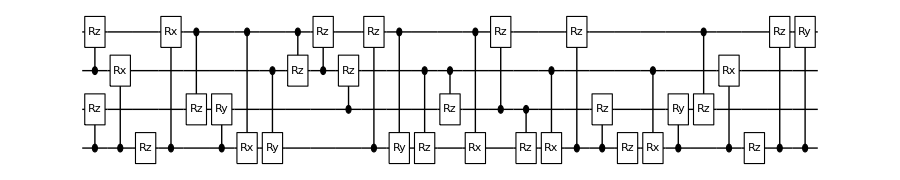

cost=8.44959×10^-8; ngates=30

runtime= 11.5435 minutes

cost=8.44959×10^-8 ;dist=0.000468679; globalphase=0.0486212

Cycle1, @Sat 19 Mar 2022 23:37:28, fev:473, <E>: 0.001997687810484372 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:37:43, fev:570, <E>: 0.001997687810484372 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sat 19 Mar 2022 23:37:58, fev:680, <E>: 0.001997687810484372 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 31, 0, 0, 5}

pruning exceeds the maxcost: 1.×10^-7; cost=0.00199769

{{C_1[Rz_0[θ_50]],C_3[Rz_1[θ_47]],C_1[Ry_3[θ_38]],C_1[Rx_3[θ_37]],C_1[Ry_3[θ_35]],C_0[Rz_3[θ_48]],C_3[Rz_2[θ_14]],Rz_2[θ_13],C_1[Rz_2[θ_3]],C_2[Rz_0[θ_46]],Rz_1[θ_9],C_2[Rz_0[θ_28]],C_3[Rz_2[θ_21]],C_1[Rz_0[θ_34]],C_1[Rz_0[θ_11]],C_1[Rz_3[θ_36]],C_0[Rz_2[θ_22]],Rz_3[θ_44],C_2[Rz_0[θ_8]]},<|θ_3→0.33182,θ_8→1.10597,θ_9→0.375031,θ_11→0.645973,θ_13→-0.577697,θ_14→-0.224151,θ_21→0.573402,θ_22→0.922063,θ_28→-3.11504,θ_34→-0.614214,θ_35→-1.5708,θ_36→0.512674,θ_37→0.821989,θ_38→1.5708,θ_44→-0.609547,θ_46→1.32826,θ_47→-1.09341,θ_48→0.331818,θ_50→0.305659|>,{2,3},777,3,{merged, θsmall, metric, bruteforce}=,{0,31,0,0},Compilation is either converging or stuck. }

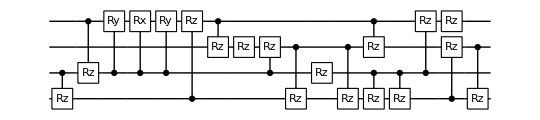

cost=0.00199769; ngates=19

runtime= 1.05277 minutes

cost=0.00199769 ;dist=0.0905743; globalphase=0.0483968

Cycle1, @Sat 19 Mar 2022 23:38:51, fev:798, <E>: 0.001997676652665037 nansatz:14 merged-smallθ,metric,bf,gmerged: {2, 31, 3, 0, 2}

Cycle2, @Sat 19 Mar 2022 23:39:42, fev:1541, <E>: 0.0010487190451573536 nansatz:20 merged-smallθ,metric,bf,gmerged: {2, 65, 3, 0, 4}

Cycle3, @Sat 19 Mar 2022 23:40:47, fev:2249, <E>: 0.00002129994251764966 nansatz:22 merged-smallθ,metric,bf,gmerged: {2, 96, 10, 0, 4}

Cycle4, @Sat 19 Mar 2022 23:43:32, fev:4243, <E>: 4.767808025052389e-7 nansatz:27 merged-smallθ,metric,bf,gmerged: {2, 131, 10, 0, 4}

Cycle5, @Sat 19 Mar 2022 23:46:33, fev:6211, <E>: 2.1893495028013632e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {2, 165, 10, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 6

Cycle6, @Sat 19 Mar 2022 23:47:00, fev:6362, <E>: 2.1893495028013632e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {2, 165, 10, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 7

Cycle7, @Sat 19 Mar 2022 23:47:25, fev:6483, <E>: 2.1893495028013632e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {2, 165, 10, 0, 6}

I'm slowing down. Number of gates is increased to 70 @cycle 8

Cycle8, @Sat 19 Mar 2022 23:48:02, fev:6625, <E>: 2.1893495028013632e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {2, 165, 10, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=2.18935×10^-7

{{C_3[Rz_1[θ_172]],Rz_0[θ_179],C_3[Ry_1[θ_173]],C_2[Rx_1[θ_177]],C_2[Rx_1[θ_180]],C_3[Ry_1[θ_188]],C_3[Rz_0[θ_192]],C_3[Ry_1[θ_199]],C_2[Rx_0[θ_200]],C_3[Rz_1[θ_204]],Rz_3[θ_205],C_0[Rz_3[θ_206]],C_0[Rz_2[θ_208]],C_2[Rx_0[θ_138]],C_2[Ry_0[θ_141]],C_1[Rz_2[θ_158]],C_2[Rx_0[θ_163]],C_0[Ry_3[θ_127]],C_2[Ry_1[θ_59]],C_2[Rx_0[θ_61]],C_0[Rx_2[θ_78]],C_2[Rz_0[θ_93]],C_1[Rz_2[θ_92]],C_0[Rz_3[θ_128]],C_3[Rz_2[θ_112]],C_0[Rx_2[θ_45]],C_2[Rx_0[θ_23]],C_1[Rz_0[θ_95]],C_0[Rz_3[θ_13]],C_2[Ry_1[θ_71]],C_1[Rz_2[θ_58]],C_1[Rz_0[θ_46]],C_0[Rx_3[θ_54]]},<|θ_13→3.33111,θ_23→-3.14159,θ_45→-0.308207,θ_46→0.337377,θ_54→-3.14159,θ_58→7.0058,θ_59→3.14091,θ_61→3.14159,θ_71→-3.14085,θ_78→0.308185,θ_92→-5.68528,θ_93→11.3629,θ_95→6.26934,θ_112→-5.68528,θ_127→-3.14159,θ_128→0.348825,θ_138→-1.57086,θ_141→0.962207,θ_158→-6.67394,θ_163→-1.57049,θ_172→-0.00659569,θ_173→0.0950491,θ_177→-0.224449,θ_179→1.7123,θ_180→0.224223,θ_188→-0.0202244,θ_192→0.87018,θ_199→-0.0748065,θ_200→3.14132,θ_204→0.24785,θ_205→-2.52446,θ_206→-0.58406,θ_208→-1.08045|>,{6,7,8},6959,8,{merged, θsmall, metric, bruteforce}=,{2,165,10,0},Compilation is either converging or stuck. }

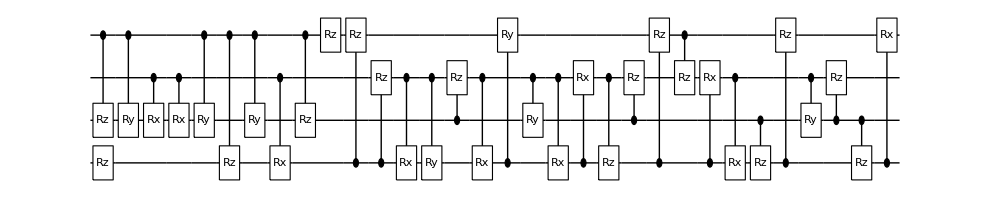

cost=2.18935×10^-7; ngates=33

runtime= 10.2537 minutes

cost=2.18935×10^-7 ;dist=0.00070036; globalphase=0.0485392

Cycle1, @Sat 19 Mar 2022 23:48:45, fev:488, <E>: 0.0019976992581713926 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 37, 0, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:48:56, fev:569, <E>: 0.0019976992581713926 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 37, 0, 0, 4}

Cycle3, @Sat 19 Mar 2022 23:49:37, fev:1046, <E>: 0.0010003315033152438 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 66, 11, 0, 4}

Cycle4, @Sat 19 Mar 2022 23:50:42, fev:1818, <E>: 0.0006688927684166401 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 106, 17, 0, 4}

Cycle5, @Sat 19 Mar 2022 23:51:41, fev:2571, <E>: 0.000036262365840755706 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 147, 28, 0, 7}

Cycle6, @Sat 19 Mar 2022 23:53:03, fev:3544, <E>: 2.1536594227988815e-6 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 186, 35, 0, 14}

Cycle7, @Sat 19 Mar 2022 23:54:09, fev:4442, <E>: 3.4809900006926853e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 221, 44, 2, 14}

Cycle8, @Sat 19 Mar 2022 23:56:36, fev:6292, <E>: 2.0606171247106175e-7 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 260, 44, 2, 16}

I'm slowing down. Number of gates is increased to 58 @cycle 9

Cycle9, @Sat 19 Mar 2022 23:57:02, fev:6417, <E>: 2.0606171247106175e-7 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 260, 44, 2, 17}

I'm slowing down. Number of gates is increased to 70 @cycle 10

Cycle10, @Sat 19 Mar 2022 23:57:36, fev:6547, <E>: 2.0606171247106175e-7 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 260, 44, 2, 20}

pruning exceeds the maxcost: 1.×10^-7; cost=2.06062×10^-7

{{Rz_0[θ_313],C_2[Rx_3[θ_317]],C_0[Rz_1[θ_281]],C_2[Ry_3[θ_296]],Rz_2[θ_167],C_3[Rz_2[θ_243]],C_3[Ry_0[θ_80]],C_0[Rz_2[θ_334]],C_3[Ry_1[θ_108]],C_3[Ry_2[θ_17]],C_0[Rx_3[θ_292]],C_2[Rz_0[θ_276]],C_2[Rx_3[θ_306]],C_1[Rx_3[θ_303]],C_1[Rz_3[θ_307]],C_1[Rz_0[θ_245]],C_0[Rz_3[θ_154]],C_1[Rz_2[θ_165]],C_2[Rz_3[θ_149]],C_1[Ry_3[θ_131]],C_3[Ry_2[θ_321]],C_3[Ry_2[θ_23]],C_2[Rz_1[θ_289]],C_3[Ry_0[θ_66]],Rz_1[θ_308],Rz_0[θ_319],C_2[Rz_3[θ_330]],C_1[Rz_0[θ_258]],C_3[Ry_1[θ_58]],C_3[Ry_1[θ_326]],C_2[Rz_1[θ_305]],C_3[Rz_0[θ_257]]},<|θ_17→-3.14159,θ_23→3.28938,θ_58→2.86301,θ_66→-3.14159,θ_80→3.14159,θ_108→-3.14159,θ_131→0.10568,θ_149→-2.02016,θ_154→2.01866,θ_165→-1.30131,θ_167→-0.867127,θ_243→0.1635,θ_245→0.749153,θ_257→1.32215,θ_258→-0.00304559,θ_276→0.241248,θ_281→-0.411641,θ_289→0.00305031,θ_292→0.000919748,θ_296→3.14159,θ_303→-0.105842,θ_305→1.63317,θ_306→-0.0010211,θ_307→1.56485,θ_308→-0.12215,θ_313→0.0241432,θ_317→3.14159,θ_319→0.152699,θ_321→-0.147783,θ_326→0.278583,θ_330→2.0256,θ_334→0.0005117|>,{2,9,10},6901,10,{merged, θsmall, metric, bruteforce}=,{0,260,44,2},Compilation is either converging or stuck. }

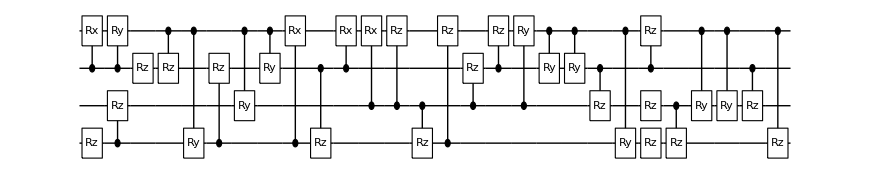

cost=2.06062×10^-7; ngates=32

runtime= 9.66293 minutes

cost=2.06062×10^-7 ;dist=0.000711725; globalphase=0.0485948

Cycle1, @Sat 19 Mar 2022 23:58:50, fev:584, <E>: 0.0019976791168071495 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 27, 0, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sat 19 Mar 2022 23:59:10, fev:702, <E>: 0.0019976791168071495 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 27, 0, 0, 0}

Cycle3, @Sun 20 Mar 2022 00:01:06, fev:2081, <E>: 0.0010186405388613595 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 58, 11, 0, 0}

Cycle4, @Sun 20 Mar 2022 00:02:14, fev:2703, <E>: 0.0005213062714946037 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 106, 19, 0, 3}

Cycle5, @Sun 20 Mar 2022 00:02:49, fev:3139, <E>: 1.7701413280724054e-6 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 147, 26, 0, 8}

Cycle6, @Sun 20 Mar 2022 00:03:43, fev:4423, <E>: 4.6568730538432135e-7 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 182, 33, 0, 11}

Cycle7, @Sun 20 Mar 2022 00:05:42, fev:5913, <E>: 2.1649184844818592e-7 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 220, 33, 0, 12}

I'm slowing down. Number of gates is increased to 58 @cycle 8

Cycle8, @Sun 20 Mar 2022 00:06:07, fev:6019, <E>: 2.1649184844818592e-7 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 220, 33, 0, 13}

I'm slowing down. Number of gates is increased to 70 @cycle 9

Cycle9, @Sun 20 Mar 2022 00:06:46, fev:6156, <E>: 2.1649184844818592e-7 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 220, 33, 0, 13}

pruning exceeds the maxcost: 1.×10^-7; cost=2.16492×10^-7

{{C_0[Rz_1[θ_279]],C_1[Rx_3[θ_58]],C_2[Rx_0[θ_42]],Rz_0[θ_21],C_2[Rx_1[θ_94]],C_0[Ry_2[θ_207]],C_3[Rz_1[θ_37]],C_0[Rx_2[θ_199]],C_1[Ry_2[θ_245]],C_0[Rz_2[θ_145]],C_2[Rx_1[θ_264]],C_2[Rx_1[θ_243]],C_1[Rz_3[θ_259]],C_3[Ry_2[θ_158]],C_1[Ry_2[θ_272]],C_3[Ry_0[θ_230]],C_0[Ry_2[θ_290]],C_3[Rx_0[θ_260]],C_3[Rx_0[θ_251]],C_2[Rz_0[θ_278]],C_2[Rz_3[θ_256]],C_0[Ry_2[θ_213]],C_1[Rz_2[θ_271]],C_3[Ry_0[θ_231]],C_2[Rx_1[θ_73]],C_3[Rz_0[θ_263]],C_1[Ry_3[θ_84]],C_2[Ry_0[θ_22]],C_1[Rz_2[θ_249]],C_1[Rz_0[θ_267]],C_0[Rz_3[θ_126]],C_0[Rz_2[θ_275]],C_3[Rz_2[θ_191]],C_1[Rz_3[θ_8]],C_2[Rz_0[θ_210]]},<|θ_8→-3.02604,θ_21→-0.811842,θ_22→3.14159,θ_37→0.151567,θ_42→3.14159,θ_58→-3.14159,θ_73→3.14159,θ_84→3.14159,θ_94→-3.14159,θ_126→0.331846,θ_145→-2.94221,θ_158→-0.0894641,θ_191→0.323495,θ_199→0.0174928,θ_207→0.088935,θ_210→-0.874538,θ_213→0.753688,θ_230→3.14159,θ_231→-3.14159,θ_243→0.74164,θ_245→-0.00119756,θ_249→0.483405,θ_251→-0.11596,θ_256→0.000574083,θ_259→-0.126253,θ_260→0.11596,θ_263→-0.000580557,θ_264→-0.74164,θ_267→0.731439,θ_271→-0.0507468,θ_272→0.00121466,θ_275→2.63278,θ_278→-0.000584474,θ_279→-0.394075,θ_290→-0.664235|>,{2,8,9},6527,9,{merged, θsmall, metric, bruteforce}=,{0,220,33,0},Compilation is either converging or stuck. }

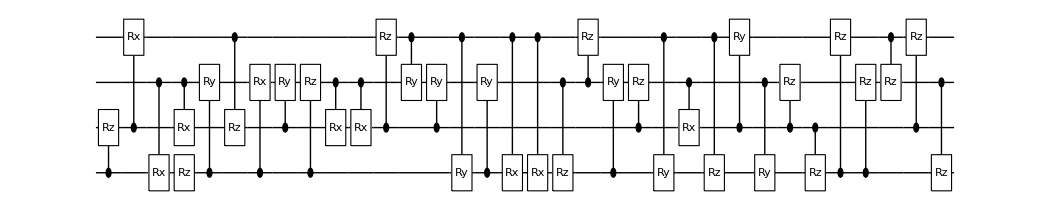

cost=2.16492×10^-7; ngates=35

runtime= 9.11129 minutes

cost=2.16492×10^-7 ;dist=0.000635473; globalphase=0.0486219

Cycle1, @Sun 20 Mar 2022 00:08:29, fev:1191, <E>: 0.0016456126823893857 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 26, 1, 0, 0}

Cycle2, @Sun 20 Mar 2022 00:09:33, fev:1830, <E>: 0.0010385396301867411 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 66, 4, 0, 0}

Cycle3, @Sun 20 Mar 2022 00:10:16, fev:2348, <E>: 0.0010007890699210709 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 99, 11, 0, 0}

Cycle4, @Sun 20 Mar 2022 00:10:59, fev:2931, <E>: 0.0009997475589221816 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 131, 17, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 5

Cycle5, @Sun 20 Mar 2022 00:11:20, fev:3058, <E>: 0.0009997475589221816 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 131, 17, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 6

Cycle6, @Sun 20 Mar 2022 00:11:38, fev:3167, <E>: 0.0009997475589221816 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 131, 17, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=0.000999748

{{Rz_1[θ_56],C_1[Rz_2[θ_60]],C_0[Rz_2[θ_157]],C_2[Rz_0[θ_63]],Rz_2[θ_64],C_1[Rz_0[θ_80]],C_3[Rx_0[θ_3]],C_3[Rz_1[θ_5]],Ry_3[θ_9],C_1[Rx_3[θ_19]],C_3[Rz_1[θ_24]],Rx_3[θ_26],C_2[Ry_1[θ_30]],C_0[Ry_2[θ_158]],C_3[Ry_2[θ_31]],C_3[Rz_1[θ_139]],C_2[Ry_1[θ_34]],C_1[Rx_3[θ_35]],Rz_2[θ_97],C_3[Rx_0[θ_45]],C_0[Rz_1[θ_135]],C_0[Rz_3[θ_106]]},<|θ_3→3.14159,θ_5→-3.01592,θ_9→-1.5708,θ_19→-0.115634,θ_24→3.1416,θ_26→1.5708,θ_30→-3.14159,θ_31→-0.0898416,θ_34→3.14159,θ_35→-3.1416,θ_45→-3.14159,θ_56→-0.204871,θ_60→0.680701,θ_63→-0.740273,θ_64→-2.37525,θ_80→0.396616,θ_97→1.76784,θ_106→0.33197,θ_135→-0.059275,θ_139→0.348835,θ_157→0.981495,θ_158→0.000744552|>,{5,6},3339,6,{merged, θsmall, metric, bruteforce}=,{0,131,17,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000999748; ngates=22

runtime= 4.4458 minutes

cost=0.000999748 ;dist=0.0456806; globalphase=0.0485642

Cycle1, @Sun 20 Mar 2022 00:12:00, fev:374, <E>: 0.001997681151593489 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 32, 0, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sun 20 Mar 2022 00:12:11, fev:460, <E>: 0.001997681151593489 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 32, 0, 0, 7}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sun 20 Mar 2022 00:12:23, fev:549, <E>: 0.001997681151593489 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 32, 0, 0, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=0.00199768

{{C_3[Rz_0[θ_28]],Rz_3[θ_36],C_0[Rz_2[θ_47]],C_3[Rz_0[θ_33]],C_3[Rz_2[θ_41]],C_0[Rz_2[θ_38]],C_2[Rz_0[θ_14]],C_2[Rz_1[θ_16]],C_1[Rz_0[θ_19]],Rz_1[θ_2],C_1[Rz_3[θ_34]],C_3[Rz_2[θ_6]],C_2[Rz_1[θ_29]],C_2[Rz_0[θ_42]],Rz_1[θ_44],C_2[Rz_3[θ_25]],C_2[Rz_0[θ_4]],C_3[Rz_2[θ_9]]},<|θ_2→-1.26185,θ_4→-0.233833,θ_6→-0.0227367,θ_9→-0.976181,θ_14→-1.16968,θ_16→-0.266008,θ_19→0.337321,θ_25→1.15494,θ_28→0.378326,θ_29→0.597878,θ_33→-0.0465223,θ_34→0.240894,θ_36→-0.474198,θ_38→0.244938,θ_41→0.192757,θ_42→0.39109,θ_44→0.92412,θ_47→1.00866|>,{2,3},624,3,{merged, θsmall, metric, bruteforce}=,{0,32,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.00199768; ngates=18

runtime= 0.701284 minutes

cost=0.00199768 ;dist=0.0905743; globalphase=0.0486571

Cycle1, @Sun 20 Mar 2022 00:13:19, fev:950, <E>: 0.0019976721932204455 nansatz:20 merged-smallθ,metric,bf,gmerged: {1, 29, 0, 0, 1}

Cycle2, @Sun 20 Mar 2022 00:14:02, fev:1485, <E>: 0.0010063215661691993 nansatz:18 merged-smallθ,metric,bf,gmerged: {1, 60, 10, 0, 2}

Cycle3, @Sun 20 Mar 2022 00:15:04, fev:2329, <E>: 0.0003231311177627205 nansatz:21 merged-smallθ,metric,bf,gmerged: {1, 92, 14, 0, 5}

Cycle4, @Sun 20 Mar 2022 00:15:57, fev:2986, <E>: 4.12260730664471e-7 nansatz:22 merged-smallθ,metric,bf,gmerged: {1, 123, 22, 0, 8}

Cycle5, @Sun 20 Mar 2022 00:17:06, fev:4129, <E>: 1.6863309570958052e-7 nansatz:25 merged-smallθ,metric,bf,gmerged: {1, 160, 22, 0, 8}

I'm slowing down. Number of gates is increased to 48 @cycle 6

Cycle6, @Sun 20 Mar 2022 00:17:28, fev:4246, <E>: 1.6863309570958052e-7 nansatz:25 merged-smallθ,metric,bf,gmerged: {1, 160, 22, 0, 10}

I'm slowing down. Number of gates is increased to 58 @cycle 7

Cycle7, @Sun 20 Mar 2022 00:17:59, fev:4378, <E>: 1.6863309570958052e-7 nansatz:25 merged-smallθ,metric,bf,gmerged: {1, 160, 22, 0, 13}

I'm slowing down. Number of gates is increased to 70 @cycle 8

Cycle8, @Sun 20 Mar 2022 00:19:02, fev:4598, <E>: 1.6863309570958052e-7 nansatz:25 merged-smallθ,metric,bf,gmerged: {1, 160, 22, 0, 15}

pruning exceeds the maxcost: 1.×10^-7; cost=1.68633×10^-7

{{C_0[Rz_1[θ_67]],C_2[Rz_3[θ_37]],C_1[Rx_0[θ_26]],C_1[Ry_2[θ_73]],C_3[Rz_1[θ_99]],C_2[Rz_1[θ_149]],C_1[Ry_3[θ_15]],Rz_3[θ_102],C_3[Rz_2[θ_125]],C_3[Rx_1[θ_176]],C_1[Rz_0[θ_180]],C_3[Ry_1[θ_161]],C_2[Rz_1[θ_51]],C_2[Rx_1[θ_207]],C_2[Rz_3[θ_178]],C_1[Rz_0[θ_129]],C_3[Ry_1[θ_89]],C_3[Ry_1[θ_208]],C_3[Rz_0[θ_209]],C_1[Ry_2[θ_56]],Rz_2[θ_95],C_1[Ry_0[θ_87]],C_1[Rz_3[θ_163]],C_0[Rz_2[θ_202]],C_1[Ry_3[θ_9]]},<|θ_9→-3.14159,θ_15→3.14159,θ_26→3.14159,θ_37→0.0516948,θ_51→-3.48139,θ_56→3.14159,θ_67→1.01188,θ_73→-3.14159,θ_87→3.14159,θ_89→-0.0636658,θ_95→-1.66425,θ_99→2.17923,θ_102→0.852094,θ_125→-0.331858,θ_129→-2.91478,θ_149→-0.0525707,θ_161→0.0153158,θ_163→-0.395014,θ_176→0.0898345,θ_178→0.62899,θ_180→0.115842,θ_202→0.241248,θ_207→0.00076216,θ_208→-0.0270788,θ_209→0.331849|>,{6,7,8},4826,8,{merged, θsmall, metric, bruteforce}=,{1,160,22,0},I keep failing to lower the energy. }

-Graphics-

cost=1.68633×10^-7; ngates=25

runtime= 6.7632 minutes

cost=1.68633×10^-7 ;dist=0.000616066; globalphase=0.0485803

Cycle1, @Sun 20 Mar 2022 00:19:48, fev:577, <E>: 0.001997679308060052 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 32, 4, 1, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Sun 20 Mar 2022 00:20:01, fev:680, <E>: 0.001997679308060052 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 32, 4, 1, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Sun 20 Mar 2022 00:20:17, fev:781, <E>: 0.001997679308060052 nansatz:13 merged-smallθ,metric,bf,gmerged: {0, 32, 4, 1, 7}

pruning exceeds the maxcost: 1.×10^-7; cost=0.00199768

{{C_3[Rz_0[θ_1]],C_3[Rz_1[θ_3]],C_0[Rx_1[θ_6]],C_3[Rz_2[θ_14]],C_0[Rz_1[θ_19]],C_2[Rz_0[θ_21]],C_0[Rx_1[θ_23]],Rz_0[θ_27],C_1[Rz_2[θ_29]],C_2[Rz_3[θ_36]],C_0[Ry_1[θ_40]],Rz_3[θ_42],Rz_1[θ_48]},<|θ_1→0.331862,θ_3→0.241251,θ_6→-0.00394567,θ_14→0.11536,θ_19→0.337432,θ_21→0.24125,θ_23→0.00388332,θ_27→-0.458231,θ_29→0.332,θ_36→0.233473,θ_40→0.00133296,θ_42→0.106957,θ_48→-0.460987|>,{2,3},833,3,{merged, θsmall, metric, bruteforce}=,{0,32,4,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.00199768; ngates=13

runtime= 1.08576 minutes

cost=0.00199768 ;dist=0.0905742; globalphase=0.0485558

Cycle1, @Sun 20 Mar 2022 00:21:38, fev:1309, <E>: 0.022487974858541926 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 22, 4, 0, 2}

Cycle2, @Sun 20 Mar 2022 00:22:48, fev:2078, <E>: 0.012184229534325075 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 57, 7, 0, 3}

Cycle3, @Sun 20 Mar 2022 00:23:48, fev:2727, <E>: 0.01180657860122436 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 87, 15, 0, 6}

Cycle4, @Sun 20 Mar 2022 00:25:54, fev:4261, <E>: 0.01140837397877692 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 120, 20, 0, 6}

Cycle5, @Sun 20 Mar 2022 00:28:24, fev:5822, <E>: 0.0039963818121662165 nansatz:38 merged-smallθ,metric,bf,gmerged: {0, 146, 26, 0, 7}

Cycle6, @Sun 20 Mar 2022 00:31:18, fev:7457, <E>: 0.0004727413476079967 nansatz:38 merged-smallθ,metric,bf,gmerged: {0, 180, 32, 0, 8}

Cycle7, @Sun 20 Mar 2022 00:34:10, fev:9231, <E>: 0.000012103443284505744 nansatz:39 merged-smallθ,metric,bf,gmerged: {0, 214, 37, 0, 9}

{{C_1[Ry_2[θ_16]],C_3[Rz_2[θ_176]],C_1[Rz_0[θ_259]],C_0[Ry_3[θ_172]],C_0[Rz_1[θ_294]],C_1[Rx_0[θ_8]],C_2[Rz_1[θ_243]],C_3[Rz_2[θ_329]],Ry_1[θ_178],C_1[Rz_2[θ_307]],C_1[Rz_3[θ_197]],C_0[Ry_1[θ_281]],C_3[Rz_2[θ_305]],C_0[Ry_1[θ_296]],Ry_1[θ_313],C_1[Ry_0[θ_41]],C_0[Ry_3[θ_196]],Rz_1[θ_28],C_2[Rz_1[θ_327]],Ry_3[θ_47],C_1[Rz_2[θ_323]],C_2[Rz_0[θ_216]],C_0[Rx_1[θ_11]],C_2[Rz_1[θ_44]],C_0[Rx_1[θ_1]],C_2[Rx_3[θ_144]],C_1[Rx_2[θ_21]],C_2[Rx_3[θ_14]],Ry_3[θ_24],C_3[Rz_0[θ_293]],C_1[Rx_3[θ_58]],C_1[Rx_0[θ_59]],C_2[Rx_1[θ_65]],Ry_2[θ_202],C_0[Rx_2[θ_156]],C_2[Rz_3[θ_315]],C_0[Rz_2[θ_284]],C_2[Rx_1[θ_298]],C_1[Rx_3[θ_84]],Rz_2[θ_264],C_1[Rz_3[θ_194]],C_0[Rz_3[θ_203]],C_1[Ry_0[θ_85]],C_3[Rz_2[θ_319]],C_0[Rz_1[θ_90]],C_2[Rz_0[θ_209]]},<|θ_1→-3.14159,θ_8→-3.14159,θ_11→3.14159,θ_14→2.14352,θ_16→-3.14159,θ_21→-3.14159,θ_24→-1.5708,θ_28→-2.00916,θ_41→-3.14159,θ_44→0.034478,θ_47→1.5708,θ_58→3.14159,θ_59→-3.14159,θ_65→3.14159,θ_84→-3.14159,θ_85→-3.14159,θ_90→3.55806,θ_144→-2.33668,θ_156→-0.412024,θ_172→3.14159,θ_176→4.4488,θ_178→-0.149007,θ_194→-7.36202,θ_196→-3.14159,θ_197→-3.08593,θ_202→0.31566,θ_203→3.0754,θ_209→0.930484,θ_216→0.95407,θ_243→1.96172,θ_259→4.71766,θ_264→1.88136,θ_281→-0.458403,θ_284→-0.887017,θ_293→-1.75861,θ_294→-0.608577,θ_296→0.244409,θ_298→-3.14159,θ_305→-0.309197,θ_307→0.00232878,θ_313→-0.275249,θ_315→-2.04379,θ_319→-0.748272,θ_323→-2.63699,θ_327→4.01969,θ_329→0.309214|>,{},13421,8,{merged, θsmall, metric, bruteforce}=,{0,247,37,0},Circuit within target precision is found}

-Graphics-

cost=5.86751×10^-8; ngates=46

runtime= 19.089 minutes

cost=5.86751×10^-8 ;dist=0.000348894; globalphase=4.90655

Cycle1, @Sun 20 Mar 2022 00:40:10, fev:674, <E>: 0.022457213258970876 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 25, 7, 0, 0}

Cycle2, @Sun 20 Mar 2022 00:40:44, fev:1334, <E>: 0.012009932119119715 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 58, 9, 0, 2}

Cycle3, @Sun 20 Mar 2022 00:41:56, fev:2263, <E>: 0.011737382810881991 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 96, 9, 0, 5}

Cycle4, @Sun 20 Mar 2022 00:42:44, fev:2840, <E>: 0.011381529027130854 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 126, 19, 0, 7}

Cycle5, @Sun 20 Mar 2022 00:43:22, fev:3508, <E>: 0.00713381198973706 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 158, 26, 0, 10}

Cycle6, @Sun 20 Mar 2022 00:47:11, fev:6749, <E>: 0.007079924392252135 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 184, 31, 0, 11}

Cycle7, @Sun 20 Mar 2022 00:48:30, fev:7855, <E>: 0.00500560171922837 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 225, 35, 0, 13}

Cycle8, @Sun 20 Mar 2022 00:50:03, fev:9288, <E>: 0.0008748710167649776 nansatz:31 merged-smallθ,metric,bf,gmerged: {0, 260, 38, 0, 13}

Cycle9, @Sun 20 Mar 2022 00:53:08, fev:11541, <E>: 0.000032378480207650995 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 290, 44, 0, 14}

{{C_0[Rz_3[θ_345]],C_2[Rz_0[θ_368]],C_3[Rx_1[θ_59]],C_3[Rx_0[θ_63]],C_3[Rx_2[θ_64]],C_1[Rx_3[θ_369]],C_3[Rz_0[θ_267]],C_3[Rz_1[θ_374]],C_2[Rz_1[θ_388]],C_2[Rx_3[θ_156]],C_2[Ry_3[θ_394]],C_2[Rz_3[θ_335]],C_0[Rz_3[θ_201]],C_0[Rz_2[θ_397]],C_1[Rz_3[θ_385]],C_1[Rx_3[θ_407]],C_0[Rz_3[θ_192]],C_2[Rz_0[θ_381]],Rz_3[θ_373],C_3[Rz_0[θ_341]],C_1[Rz_3[θ_380]],C_2[Rx_3[θ_274]],C_3[Rx_0[θ_122]],C_0[Ry_2[θ_28]],C_2[Rz_3[θ_121]],Rz_0[θ_317],Ry_2[θ_403],C_3[Rx_1[θ_100]],Rz_2[θ_208],C_1[Rz_0[θ_264]],Rx_2[θ_269],C_2[Rz_0[θ_275]],C_3[Rz_2[θ_36]],Rx_2[θ_238],Ry_2[θ_382]},<|θ_28→-3.14162,θ_36→-3.14151,θ_59→-3.14159,θ_63→-3.14159,θ_64→3.14161,θ_100→-3.14159,θ_121→1.11825,θ_122→-3.14159,θ_156→0.30326,θ_192→2.69273,θ_201→-5.30795,θ_208→1.57056,θ_238→2.12658,θ_264→1.34954,θ_267→4.16157,θ_269→-0.778923,θ_274→0.348984,θ_275→3.14161,θ_317→2.60187,θ_335→-0.649437,θ_341→-3.6677,θ_345→0.543167,θ_368→2.52007,θ_369→-0.424733,θ_373→7.73088,θ_374→-2.29234,θ_380→-12.1292,θ_381→1.86351,θ_382→-1.57091,θ_385→3.22713,θ_388→1.32738,θ_394→0.175589,θ_397→-1.39527,θ_403→0.791892,θ_407→0.424501|>,{},15341,10,{merged, θsmall, metric, bruteforce}=,{1,327,44,0},Circuit within target precision is found}

-Graphics-

cost=4.20173×10^-8; ngates=35

runtime= 18.692 minutes

cost=4.20173×10^-8 ;dist=0.000292537; globalphase=4.12115

Cycle1, @Sun 20 Mar 2022 00:59:39, fev:1290, <E>: 0.022458683826633963 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 27, 3, 0, 4}

Cycle2, @Sun 20 Mar 2022 01:00:53, fev:2633, <E>: 0.022431543543545374 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 62, 5, 0, 7}

Cycle3, @Sun 20 Mar 2022 01:05:05, fev:5992, <E>: 0.02242990214671814 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 96, 5, 0, 8}

I'm slowing down. Number of gates is increased to 48 @cycle 4

Cycle4, @Sun 20 Mar 2022 01:05:39, fev:6213, <E>: 0.02242990214671814 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 96, 5, 0, 11}

I'm slowing down. Number of gates is increased to 58 @cycle 5

Cycle5, @Sun 20 Mar 2022 01:06:22, fev:6453, <E>: 0.02242990214671814 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 96, 5, 0, 17}

Cycle6, @Sun 20 Mar 2022 01:08:08, fev:7288, <E>: 0.018776751035208705 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 162, 8, 0, 18}

Cycle7, @Sun 20 Mar 2022 01:09:18, fev:7990, <E>: 0.011982713887232155 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 206, 20, 0, 21}

Cycle8, @Sun 20 Mar 2022 01:11:11, fev:9157, <E>: 0.0015032084223838282 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 253, 25, 0, 21}

Cycle9, @Sun 20 Mar 2022 01:13:09, fev:10100, <E>: 0.00012100358446642812 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 290, 39, 0, 21}

{{C_1[Rz_3[θ_365]],C_3[Rz_2[θ_257]],C_1[Rx_3[θ_259]],C_0[Rx_2[θ_261]],C_3[Rz_2[θ_363]],C_0[Rz_1[θ_335]],C_1[Ry_2[θ_375]],C_3[Rz_2[θ_398]],Rz_2[θ_404],Rz_3[θ_396],C_1[Rz_2[θ_320]],C_0[Ry_1[θ_264]],C_2[Rz_0[θ_407]],C_1[Rz_2[θ_382]],C_0[Rx_2[θ_289]],C_3[Rx_0[θ_374]],C_3[Rz_1[θ_377]],C_0[Ry_1[θ_302]],C_1[Rx_3[θ_303]],C_1[Rz_0[θ_4]],C_0[Rz_2[θ_371]],C_1[Rz_2[θ_372]],C_2[Rz_0[θ_93]],C_3[Rx_2[θ_385]],Rz_2[θ_362],C_1[Rz_3[θ_40]],C_2[Rz_0[θ_392]],C_1[Ry_2[θ_353]],C_1[Rx_0[θ_137]],C_3[Ry_1[θ_158]],C_1[Rx_3[θ_207]],C_3[Ry_1[θ_162]],C_0[Rz_3[θ_348]],C_1[Rx_0[θ_177]],C_3[Rx_2[θ_181]],C_2[Rz_3[θ_349]]},<|θ_4→-2.21325,θ_40→-0.477809,θ_93→0.0141994,θ_137→3.14159,θ_158→-3.14159,θ_162→3.14159,θ_177→-3.14159,θ_181→3.14159,θ_207→-0.418493,θ_257→-0.767155,θ_259→3.14159,θ_261→3.14159,θ_264→-3.14159,θ_289→-3.14159,θ_302→3.14159,θ_303→-3.14159,θ_320→-2.73384,θ_335→4.8901,θ_348→-0.0611737,θ_349→5.30404,θ_353→3.14159,θ_362→1.5402,θ_363→-0.557237,θ_365→3.32739,θ_371→-8.96139,θ_372→-4.72279,θ_374→0.418562,θ_375→-3.14159,θ_377→1.32738,θ_382→2.10693,θ_385→-3.14159,θ_392→0.557209,θ_396→-2.1993,θ_398→0.0218328,θ_404→0.552162,θ_407→0.209375|>,{4,5},13648,10,{merged, θsmall, metric, bruteforce}=,{0,334,49,1},Circuit within target precision is found}

-Graphics-

cost=1.61684×10^-8; ngates=36

runtime= 21.0647 minutes

cost=1.61684×10^-8 ;dist=0.000248408; globalphase=4.90657

Cycle1, @Sun 20 Mar 2022 01:20:58, fev:1375, <E>: 0.02247246965182259 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 16, 6, 0, 3}

Cycle2, @Sun 20 Mar 2022 01:24:25, fev:3421, <E>: 0.012224154123402942 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 62, 7, 0, 3}

Cycle3, @Sun 20 Mar 2022 01:25:34, fev:4182, <E>: 0.008048047627124966 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 94, 11, 0, 5}

Cycle4, @Sun 20 Mar 2022 01:30:22, fev:8315, <E>: 0.007900324654543378 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 121, 15, 0, 5}

Cycle5, @Sun 20 Mar 2022 01:34:55, fev:11009, <E>: 0.0009020463460712724 nansatz:38 merged-smallθ,metric,bf,gmerged: {0, 155, 16, 0, 8}

Cycle6, @Sun 20 Mar 2022 01:39:25, fev:13841, <E>: 0.0000665352411690634 nansatz:38 merged-smallθ,metric,bf,gmerged: {0, 193, 18, 0, 9}

{{C_3[Rz_1[θ_274]],C_0[Rz_3[θ_276]],C_1[Ry_0[θ_278]],C_2[Rz_1[θ_290]],C_2[Rz_3[θ_218]],C_3[Ry_1[θ_55]],C_1[Rx_2[θ_202]],C_2[Ry_3[θ_204]],C_3[Rz_2[θ_59]],C_2[Rx_1[θ_177]],C_2[Rz_3[θ_61]],C_1[Rx_3[θ_179]],C_3[Rz_0[θ_67]],C_2[Rx_1[θ_194]],C_1[Rx_2[θ_188]],C_3[Ry_2[θ_71]],C_1[Rx_3[θ_72]],C_3[Rz_0[θ_127]],C_1[Ry_2[θ_195]],C_2[Ry_3[θ_114]],C_1[Rz_0[θ_207]],C_1[Ry_2[θ_175]],C_0[Rz_3[θ_88]],C_1[Rz_3[θ_233]],Rx_1[θ_15],C_3[Rz_0[θ_201]],C_2[Rx_3[θ_208]],C_3[Rz_0[θ_130]],C_1[Rz_3[θ_187]],Ry_1[θ_36],C_3[Rz_2[θ_174]],C_0[Rz_1[θ_206]],C_2[Rz_3[θ_139]],Rz_0[θ_150],C_1[Ry_0[θ_160]],C_1[Rz_2[θ_200]],C_1[Rx_2[θ_172]],C_3[Rz_2[θ_209]],C_0[Rz_2[θ_168]]},<|θ_15→-1.5708,θ_36→-4.71239,θ_55→3.14159,θ_59→3.14161,θ_61→-3.14163,θ_67→-2.48067,θ_71→-3.14159,θ_72→-3.33027,θ_88→9.42468,θ_114→2.70057,θ_127→-7.11325,θ_130→2.42433,θ_139→0.952506,θ_150→3.03429,θ_160→-9.42478,θ_168→0.964994,θ_172→-3.14159,θ_174→6.54823,θ_175→-3.14159,θ_177→-3.14159,θ_179→-0.401175,θ_187→-3.1416,θ_188→-3.47094,θ_194→3.14159,θ_195→-1.57079,θ_200→3.19932,θ_201→-3.14096,θ_202→1.5708,θ_204→0.401175,θ_206→2.25767,θ_207→-9.67391,θ_208→-3.58267,θ_209→5.23943,θ_218→-0.702531,θ_233→-2.30961,θ_274→0.964993,θ_276→-1.56528,θ_278→-3.14159,θ_290→-1.49139|>,{},18230,7,{merged, θsmall, metric, bruteforce}=,{0,232,18,0},Circuit within target precision is found}

-Graphics-

cost=2.89171×10^-8; ngates=39

runtime= 27.5087 minutes

cost=2.89171×10^-8 ;dist=0.000263316; globalphase=0.194148

Cycle1, @Sun 20 Mar 2022 01:47:40, fev:532, <E>: 0.02248384745884424 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 36, 0, 0, 1}

Cycle2, @Sun 20 Mar 2022 01:49:25, fev:2330, <E>: 0.02244229453184643 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 63, 4, 0, 2}

Cycle3, @Sun 20 Mar 2022 01:53:13, fev:5739, <E>: 0.022431023568536657 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 93, 9, 0, 4}

Cycle4, @Sun 20 Mar 2022 01:56:25, fev:8738, <E>: 0.02242990380828558 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 121, 20, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 5

Cycle5, @Sun 20 Mar 2022 01:57:00, fev:8960, <E>: 0.02242990380828558 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 121, 20, 0, 6}

Cycle6, @Sun 20 Mar 2022 02:02:02, fev:11936, <E>: 0.008033086438681059 nansatz:41 merged-smallθ,metric,bf,gmerged: {0, 156, 21, 0, 9}

Cycle7, @Sun 20 Mar 2022 02:12:03, fev:17738, <E>: 0.006022170735434429 nansatz:43 merged-smallθ,metric,bf,gmerged: {0, 197, 26, 0, 11}

Cycle8, @Sun 20 Mar 2022 02:15:56, fev:19830, <E>: 0.0004415260031114254 nansatz:37 merged-smallθ,metric,bf,gmerged: {0, 242, 35, 0, 13}

Cycle9, @Sun 20 Mar 2022 02:21:22, fev:22758, <E>: 0.00003939287280707582 nansatz:41 merged-smallθ,metric,bf,gmerged: {0, 281, 40, 0, 15}

{{C_0[Rz_1[θ_8]],Rz_3[θ_36],C_2[Rz_0[θ_31]],Rz_0[θ_153],C_1[Rz_2[θ_50]],C_3[Rx_0[θ_235]],C_2[Rz_3[θ_345]],C_1[Rx_0[θ_87]],C_1[Rx_3[θ_141]],C_0[Rz_3[θ_272]],C_2[Rz_0[θ_103]],C_3[Rz_2[θ_362]],C_0[Rz_1[θ_173]],C_2[Rx_1[θ_176]],C_3[Rz_0[θ_222]],Rz_0[θ_278],Rx_2[θ_177],Rz_1[θ_393],C_3[Rz_2[θ_353]],C_3[Rx_0[θ_309]],C_0[Rz_1[θ_400]],C_1[Ry_2[θ_178]],C_3[Ry_2[θ_406]],C_0[Rx_1[θ_196]],C_3[Rz_2[θ_182]],Ry_2[θ_374],C_1[Rz_2[θ_197]],C_0[Rx_2[θ_199]],Rx_2[θ_254],C_0[Rx_1[θ_205]],C_3[Ry_2[θ_273]],C_3[Rz_2[θ_303]],C_0[Ry_2[θ_297]],C_3[Ry_0[θ_209]],C_1[Ry_2[θ_210]],C_0[Rz_3[θ_265]],C_2[Rz_0[θ_213]],Rz_2[θ_383],C_3[Rx_0[θ_251]],C_0[Rz_1[θ_371]],C_2[Rx_1[θ_214]],C_1[Rx_3[θ_217]],C_0[Rz_3[θ_390]]},<|θ_8→10.7969,θ_31→-2.17653,θ_36→-8.37064,θ_50→-0.647638,θ_87→-7.85398,θ_103→-3.14162,θ_141→-3.14159,θ_153→3.52323,θ_173→-3.14158,θ_176→3.14159,θ_177→1.57078,θ_178→0.518826,θ_182→5.85269,θ_196→-3.14159,θ_197→3.21047,θ_199→3.14187,θ_205→3.14159,θ_209→-1.5708,θ_210→-3.21048,θ_213→3.14157,θ_214→-3.14159,θ_217→3.14159,θ_222→7.22715,θ_235→1.5708,θ_251→-1.5708,θ_254→-1.57087,θ_265→-3.14159,θ_272→-4.1066,θ_273→-0.293822,θ_278→-3.60306,θ_297→0.0689043,θ_303→-3.27568,θ_309→-1.5708,θ_345→1.39549,θ_353→-0.271203,θ_362→1.94019,θ_371→-0.0451857,θ_374→-0.682192,θ_383→2.36555,θ_390→1.30483,θ_393→-4.1293,θ_400→0.0451939,θ_406→1.87018|>,{5},26012,10,{merged, θsmall, metric, bruteforce}=,{0,320,47,0},Circuit within target precision is found}

-Graphics-

cost=2.45732×10^-8; ngates=43

runtime= 40.0103 minutes

cost=2.45732×10^-8 ;dist=0.000267817; globalphase=3.33573

Cycle1, @Sun 20 Mar 2022 02:28:06, fev:1390, <E>: 0.02246365296849251 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 23, 4, 0, 2}

Cycle2, @Sun 20 Mar 2022 02:29:52, fev:2669, <E>: 0.01840564369146258 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 54, 15, 0, 5}

Cycle3, @Sun 20 Mar 2022 02:31:13, fev:3551, <E>: 0.012403555575886127 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 87, 22, 0, 8}

Cycle4, @Sun 20 Mar 2022 02:32:15, fev:4387, <E>: 0.011982654157511097 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 119, 29, 0, 11}

Cycle5, @Sun 20 Mar 2022 02:33:19, fev:5109, <E>: 0.011928304938032874 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 149, 37, 0, 12}

Cycle6, @Sun 20 Mar 2022 02:35:10, fev:6665, <E>: 0.01190404900771902 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 174, 46, 0, 14}

Cycle7, @Sun 20 Mar 2022 02:38:13, fev:9168, <E>: 0.011729266873645838 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 206, 54, 0, 14}

Cycle8, @Sun 20 Mar 2022 02:42:06, fev:12317, <E>: 0.011634226811128245 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 236, 60, 0, 14}

Cycle9, @Sun 20 Mar 2022 02:44:38, fev:14606, <E>: 0.006164925903728746 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 276, 64, 0, 21}

Cycle10, @Sun 20 Mar 2022 02:46:41, fev:16029, <E>: 0.0007168173158524915 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 313, 68, 0, 21}

Cycle11, @Sun 20 Mar 2022 02:49:48, fev:18209, <E>: 0.00036835322454042974 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 342, 74, 0, 24}

Cycle12, @Sun 20 Mar 2022 02:53:02, fev:20240, <E>: 0.00034858737175147425 nansatz:37 merged-smallθ,metric,bf,gmerged: {0, 373, 80, 0, 24}

Cycle13, @Sun 20 Mar 2022 02:55:43, fev:21927, <E>: 5.689595976576811e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 414, 86, 0, 25}

Cycle14, @Sun 20 Mar 2022 02:59:01, fev:24281, <E>: 1.2012803862759824e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 445, 92, 0, 25}

{{C_0[Rz_2[θ_576]],Rz_3[θ_554],C_1[Rz_0[θ_549]],Rz_2[θ_588],C_1[Rz_3[θ_586]],C_3[Rz_0[θ_555]],C_2[Rz_3[θ_556]],C_0[Rx_1[θ_310]],C_2[Ry_3[θ_560]],C_1[Rz_2[θ_236]],Ry_1[θ_349],C_0[Rx_2[θ_41]],C_2[Rx_0[θ_508]],C_0[Rz_3[θ_487]],C_1[Rz_0[θ_27]],C_0[Rx_1[θ_157]],C_2[Rx_0[θ_113]],C_2[Rx_3[θ_367]],C_3[Rz_0[θ_574]],C_3[Rz_0[θ_405]],Rz_0[θ_598],C_3[Rz_2[θ_493]],C_0[Ry_1[θ_579]],Rz_0[θ_350],C_0[Ry_1[θ_338]],C_2[Rx_0[θ_366]],C_0[Rx_2[θ_11]],C_2[Rz_0[θ_377]],C_1[Rz_0[θ_20]],Ry_1[θ_26],C_0[Rz_1[θ_307]],C_2[Rz_1[θ_348]],C_0[Ry_3[θ_111]],C_3[Rz_1[θ_448]],C_1[Rz_3[θ_45]]},<|θ_11→-3.14159,θ_20→3.14114,θ_26→-1.57099,θ_27→-3.14115,θ_41→3.14159,θ_45→3.32951,θ_111→3.14159,θ_113→6.68857,θ_157→3.1416,θ_236→3.15982,θ_307→0.796502,θ_310→-3.14159,θ_338→-1.67092,θ_348→-1.81416,θ_349→1.57099,θ_350→-0.83965,θ_366→5.86697,θ_367→-3.14159,θ_377→-10.5546,θ_405→-4.97955,θ_448→-1.99122,θ_487→-3.15977,θ_493→-1.64655,θ_508→0.097571,θ_549→-1.10258,θ_554→1.86357,θ_555→1.32744,θ_556→-6.40111,θ_560→3.14159,θ_574→0.350812,θ_576→0.448292,θ_579→0.015136,θ_586→-0.373461,θ_588→0.670525,θ_598→-0.230794|>,{},26143,15,{merged, θsmall, metric, bruteforce}=,{0,482,92,0},Circuit within target precision is found}

-Graphics-

cost=5.47427×10^-8; ngates=35

runtime= 34.571 minutes

cost=5.47427×10^-8 ;dist=0.000489274; globalphase=4.12113

Cycle1, @Sun 20 Mar 2022 03:03:07, fev:1173, <E>: 0.022471459703046093 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 24, 0, 0, 2}

Cycle2, @Sun 20 Mar 2022 03:05:28, fev:3133, <E>: 0.022439967681936568 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 64, 3, 0, 3}

Cycle3, @Sun 20 Mar 2022 03:06:29, fev:3788, <E>: 0.022429839401681084 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 94, 13, 0, 6}

Cycle4, @Sun 20 Mar 2022 03:07:14, fev:4346, <E>: 0.02093289123113906 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 126, 20, 0, 12}

Cycle5, @Sun 20 Mar 2022 03:08:35, fev:5321, <E>: 0.010950082774194847 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 158, 27, 0, 12}

Cycle6, @Sun 20 Mar 2022 03:10:27, fev:6579, <E>: 0.00646558213923254 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 184, 36, 0, 13}

Cycle7, @Sun 20 Mar 2022 03:12:53, fev:8178, <E>: 0.0009106161316320138 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 220, 41, 0, 15}

Cycle8, @Sun 20 Mar 2022 03:15:48, fev:10317, <E>: 0.00039056064753506536 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 254, 46, 0, 15}

Cycle9, @Sun 20 Mar 2022 03:18:33, fev:12100, <E>: 0.000020403528188772668 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 289, 50, 0, 15}

Cycle10, @Sun 20 Mar 2022 03:21:09, fev:14408, <E>: 2.226123767212762e-6 nansatz:31 merged-smallθ,metric,bf,gmerged: {0, 320, 56, 0, 17}

{{C_1[Ry_2[θ_2]],C_0[Rz_3[θ_345]],C_1[Rz_0[θ_171]],C_0[Rx_3[θ_346]],C_0[Ry_1[θ_131]],C_2[Ry_0[θ_304]],C_2[Rz_0[θ_421]],Rx_0[θ_331],C_1[Ry_2[θ_244]],C_1[Rz_0[θ_305]],C_3[Ry_0[θ_450]],C_3[Rx_0[θ_368]],C_3[Rz_0[θ_252]],C_2[Ry_0[θ_294]],Rx_0[θ_336],Rz_0[θ_412],C_0[Rz_3[θ_161]],C_0[Rz_1[θ_36]],C_3[Rz_2[θ_424]],C_1[Rz_3[θ_414]],C_2[Ry_0[θ_184]],C_0[Ry_3[θ_20]],C_0[Ry_1[θ_159]],C_0[Rz_1[θ_292]],C_1[Rz_2[θ_223]],C_2[Rz_1[θ_381]],C_3[Rz_1[θ_242]],C_2[Rz_3[θ_428]],C_0[Rz_2[θ_147]],Rz_0[θ_181],C_0[Ry_2[θ_62]],C_2[Rz_3[θ_77]],C_2[Rz_1[θ_253]]},<|θ_2→-3.14159,θ_20→-3.14159,θ_36→4.7191,θ_62→-3.14159,θ_77→6.47528,θ_131→3.14159,θ_147→4.07026,θ_159→-3.14159,θ_161→1.56218,θ_171→10.9932,θ_181→-3.09263,θ_184→0.406365,θ_223→3.18632,θ_242→3.85945,θ_244→-3.14159,θ_252→3.14258,θ_253→-1.81418,θ_292→-4.92457,θ_294→2.73733,θ_304→-0.413893,θ_305→0.414424,θ_331→1.51789,θ_336→-1.51799,θ_345→-3.14648,θ_346→3.14159,θ_368→-3.03596,θ_381→-0.0968441,θ_412→-0.156002,θ_414→-2.89447,θ_421→-0.0109098,θ_424→-5.07998,θ_428→0.0630239,θ_450→0.0208918|>,{},17494,11,{merged, θsmall, metric, bruteforce}=,{0,353,61,0},Circuit within target precision is found}

-Graphics-

cost=8.46633×10^-8; ngates=33

runtime= 23.2747 minutes

cost=8.46633×10^-8 ;dist=0.000563506; globalphase=0.194135

Cycle1, @Sun 20 Mar 2022 03:27:02, fev:1807, <E>: 0.02247503055706712 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 21, 1, 0, 1}

Cycle2, @Sun 20 Mar 2022 03:28:20, fev:2692, <E>: 0.012021037853514938 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 68, 4, 0, 1}

Cycle3, @Sun 20 Mar 2022 03:29:37, fev:3589, <E>: 0.006327130957861193 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 97, 10, 0, 5}

Cycle4, @Sun 20 Mar 2022 03:31:04, fev:4657, <E>: 0.001042367968634772 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 130, 16, 0, 7}

Cycle5, @Sun 20 Mar 2022 03:33:33, fev:6562, <E>: 0.000037289479713598084 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 158, 22, 0, 14}

{{C_0[Rz_1[θ_241]],C_3[Ry_1[θ_19]],C_0[Rz_3[θ_12]],C_1[Rz_2[θ_239]],Rz_0[θ_178],C_3[Ry_2[θ_55]],C_3[Rx_0[θ_53]],C_1[Rx_3[θ_208]],C_2[Rz_3[θ_99]],C_0[Rz_3[θ_188]],Rz_3[θ_175],C_0[Ry_3[θ_163]],C_2[Ry_3[θ_139]],C_0[Rz_2[θ_125]],C_3[Rz_1[θ_52]],C_2[Rz_1[θ_97]],C_3[Rz_0[θ_217]],C_0[Rx_3[θ_84]],C_3[Rz_0[θ_242]],C_2[Rz_0[θ_179]],C_2[Ry_3[θ_176]],C_2[Rx_3[θ_68]],Rz_3[θ_249],C_1[Rx_3[θ_230]],C_3[Rx_0[θ_77]],Rz_3[θ_111],C_3[Rx_2[θ_37]],C_3[Rz_1[θ_195]],C_3[Ry_1[θ_43]],C_1[Rz_0[θ_39]],C_3[Rz_0[θ_106]],Rz_1[θ_34]},<|θ_12→2.19244,θ_19→3.14159,θ_34→-0.522631,θ_37→-3.14159,θ_39→3.9676,θ_43→-3.14159,θ_52→-1.12294,θ_53→-3.14159,θ_55→-3.14159,θ_68→0.234492,θ_77→3.14159,θ_84→-0.450573,θ_97→1.32747,θ_99→1.40061,θ_106→-1.64692,θ_111→-0.764819,θ_125→1.74565,θ_139→0.451507,θ_163→-0.450502,θ_175→-3.92766,θ_176→-0.389437,θ_178→0.619929,θ_179→-0.780642,θ_188→4.93223,θ_195→-1.16965,θ_208→0.681478,θ_217→2.01823,θ_230→0.681525,θ_239→-0.000600159,θ_241→-2.61808,θ_242→-2.01949,θ_249→1.34653|>,{},10163,6,{merged, θsmall, metric, bruteforce}=,{0,189,27,0},Circuit within target precision is found}

-Graphics-

cost=8.18709×10^-8; ngates=32

runtime= 12.3235 minutes

cost=8.18709×10^-8 ;dist=0.000414074; globalphase=0.194172

Cycle1, @Sun 20 Mar 2022 03:38:21, fev:698, <E>: 0.022492179991737693 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 15, 6, 0, 4}

Cycle2, @Sun 20 Mar 2022 03:40:40, fev:2769, <E>: 0.022441309366008078 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 49, 13, 0, 6}

Cycle3, @Sun 20 Mar 2022 03:41:57, fev:3730, <E>: 0.01635321583644056 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 84, 18, 0, 7}

Cycle4, @Sun 20 Mar 2022 03:44:10, fev:5217, <E>: 0.01209579902054847 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 117, 21, 0, 15}

Cycle5, @Sun 20 Mar 2022 03:46:50, fev:6929, <E>: 0.0010130097054835696 nansatz:40 merged-smallθ,metric,bf,gmerged: {0, 142, 24, 0, 18}

Cycle6, @Sun 20 Mar 2022 03:50:59, fev:9075, <E>: 0.0003535628186355222 nansatz:43 merged-smallθ,metric,bf,gmerged: {0, 176, 27, 0, 18}

Cycle7, @Sun 20 Mar 2022 03:55:38, fev:11257, <E>: 0.0003154034734439426 nansatz:48 merged-smallθ,metric,bf,gmerged: {0, 211, 27, 0, 23}

Cycle8, @Sun 20 Mar 2022 04:03:22, fev:15499, <E>: 0.0002578487515341177 nansatz:46 merged-smallθ,metric,bf,gmerged: {0, 247, 33, 0, 24}

Cycle9, @Sun 20 Mar 2022 04:10:11, fev:19083, <E>: 0.00004838165725462584 nansatz:47 merged-smallθ,metric,bf,gmerged: {0, 278, 40, 0, 25}

Cycle10, @Sun 20 Mar 2022 04:26:14, fev:26445, <E>: 0.00001820494903526093 nansatz:54 merged-smallθ,metric,bf,gmerged: {0, 307, 44, 0, 26}

Cycle11, @Sun 20 Mar 2022 04:37:38, fev:31447, <E>: 1.2739582444520892e-7 nansatz:53 merged-smallθ,metric,bf,gmerged: {0, 338, 54, 0, 27}

{{C_2[Rx_3[θ_376]],C_3[Rz_0[θ_388]],C_2[Rz_0[θ_414]],C_2[Ry_3[θ_392]],Rz_0[θ_26],Rz_2[θ_355],C_3[Rz_2[θ_465]],C_2[Rz_1[θ_22]],C_3[Rz_1[θ_475]],C_3[Ry_2[θ_119]],C_3[Rz_0[θ_106]],C_1[Rz_0[θ_20]],C_3[Rx_0[θ_19]],C_1[Rx_3[θ_9]],Ry_1[θ_338],C_0[Ry_1[θ_487]],C_1[Rz_2[θ_433]],Rx_1[θ_96],C_1[Ry_3[θ_17]],C_3[Ry_0[θ_24]],C_1[Rz_0[θ_425]],C_3[Rz_2[θ_432]],Rx_3[θ_169],C_1[Rx_0[θ_7]],C_3[Ry_2[θ_129]],C_2[Rx_1[θ_112]],Rz_1[θ_164],C_2[Ry_3[θ_65]],Ry_1[θ_136],Rx_2[θ_131],C_2[Rz_0[θ_471]],C_1[Rx_0[θ_51]],C_2[Ry_3[θ_90]],C_1[Rz_3[θ_473]],Rz_0[θ_480],Rz_1[θ_468],C_2[Ry_0[θ_175]],C_3[Ry_1[θ_179]],C_0[Rz_2[θ_221]],C_2[Rz_1[θ_235]],C_3[Rz_0[θ_459]],C_3[Rz_1[θ_189]],C_2[Rx_3[θ_190]],Rx_2[θ_192],C_2[Rx_3[θ_194]],C_3[Ry_1[θ_196]],Rz_2[θ_197],C_2[Ry_0[θ_207]],C_0[Rx_2[θ_263]],C_2[Rz_1[θ_272]],C_0[Rx_2[θ_279]],C_2[Rz_3[θ_289]]},<|θ_7→3.14159,θ_9→3.14159,θ_17→-3.14159,θ_19→-3.14159,θ_20→1.02641,θ_22→1.32743,θ_24→3.14159,θ_26→3.85593,θ_51→-3.14159,θ_65→-3.14159,θ_90→3.14159,θ_96→-0.801388,θ_106→-1.81418,θ_112→-8.53925,θ_119→-3.14159,θ_129→3.14159,θ_131→-1.5708,θ_136→1.12803,θ_164→7.85398,θ_169→-1.5708,θ_175→-3.14159,θ_179→-3.14159,θ_189→0.710819,θ_190→-3.14159,θ_192→1.57062,θ_194→3.14159,θ_196→3.14159,θ_197→2.62101,θ_207→3.14159,θ_221→9.31251,θ_235→-0.400341,θ_263→-3.14159,θ_272→-2.32335,θ_279→3.14159,θ_289→1.85022,θ_338→1.75753,θ_355→-4.68129,θ_376→-3.14159,θ_388→0.0627464,θ_392→-3.14159,θ_414→1.067,θ_425→0.221648,θ_432→0.221609,θ_433→-0.142227,θ_459→0.102004,θ_465→2.76606,θ_468→0.304394,θ_471→-0.101422,θ_473→0.102026,θ_475→-1.96815,θ_480→-1.5708,θ_487→-0.374466|>,{},37221,12,{merged, θsmall, metric, bruteforce}=,{0,377,55,0},Circuit within target precision is found}

-Graphics-

cost=5.33627×10^-8; ngates=52

runtime= 72.4809 minutes

cost=5.33627×10^-8 ;dist=0.000283977; globalphase=1.76493

Cycle1, @Sun 20 Mar 2022 04:51:01, fev:1058, <E>: 0.022484785878667424 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 30, 3, 1, 0}

Cycle2, @Sun 20 Mar 2022 04:51:56, fev:1855, <E>: 0.012184618111493517 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 60, 7, 1, 3}

Cycle3, @Sun 20 Mar 2022 04:53:20, fev:2921, <E>: 0.011958283154706595 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 95, 9, 1, 4}

Cycle4, @Sun 20 Mar 2022 04:54:27, fev:3860, <E>: 0.011776938945152415 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 128, 15, 1, 7}

Cycle5, @Sun 20 Mar 2022 04:55:07, fev:4586, <E>: 0.011643321005587515 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 159, 21, 1, 10}

Cycle6, @Sun 20 Mar 2022 04:56:46, fev:5836, <E>: 0.007126342853914558 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 188, 31, 1, 11}

Cycle7, @Sun 20 Mar 2022 04:58:12, fev:6812, <E>: 0.001463889857368006 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 224, 36, 1, 14}

Cycle8, @Sun 20 Mar 2022 04:59:53, fev:8153, <E>: 0.0006388691812140301 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 258, 37, 1, 17}

Cycle9, @Sun 20 Mar 2022 05:04:17, fev:10988, <E>: 0.0005908905182534507 nansatz:38 merged-smallθ,metric,bf,gmerged: {0, 286, 41, 1, 19}

Cycle10, @Sun 20 Mar 2022 05:11:50, fev:16065, <E>: 0.0005881245986040229 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 323, 47, 1, 19}

{{C_2[Rz_3[θ_334]],C_0[Rz_3[θ_340]],C_0[Rz_1[θ_426]],C_0[Rx_3[θ_291]],C_3[Rz_1[θ_295]],C_2[Rz_3[θ_424]],C_0[Rx_3[θ_304]],C_2[Rz_1[θ_318]],C_2[Rz_0[θ_323]],C_1[Rx_2[θ_60]],C_3[Ry_0[θ_56]],C_3[Ry_1[θ_71]],C_1[Ry_3[θ_236]],C_3[Rz_0[θ_282]],C_0[Rz_3[θ_266]],C_1[Rx_3[θ_415]],C_3[Rz_2[θ_212]],C_0[Ry_3[θ_420]],C_1[Rx_3[θ_72]],C_1[Rz_3[θ_449]],C_0[Ry_3[θ_428]],C_3[Ry_1[θ_74]],C_3[Ry_0[θ_84]],C_1[Rx_2[θ_90]],C_2[Rx_3[θ_42]],Rz_0[θ_377],C_1[Rz_3[θ_191]],C_2[Rz_1[θ_200]],C_2[Rx_3[θ_35]],C_1[Rx_2[θ_378]],C_1[Rz_0[θ_380]],C_2[Rz_0[θ_381]],C_1[Rx_2[θ_383]],C_1[Rz_2[θ_386]],C_1[Rz_3[θ_403]]},<|θ_35→3.14159,θ_42→-3.14159,θ_56→-3.14159,θ_60→3.14159,θ_71→3.14159,θ_72→-5.81392,θ_74→-3.14159,θ_84→3.14159,θ_90→-3.14159,θ_191→-4.49635,θ_200→8.52043,θ_212→4.47909,θ_236→-5.92114,θ_266→2.45259,θ_282→0.0415524,θ_291→3.14159,θ_295→0.32768,θ_304→-3.14159,θ_318→-7.62571,θ_323→-8.45976,θ_334→0.0406288,θ_340→1.40815,θ_377→10.8883,θ_378→3.14159,θ_380→-2.40245,θ_381→-0.0390204,θ_383→-3.14159,θ_386→-1.37143,θ_403→0.965139,θ_415→0.297041,θ_420→-4.76847,θ_424→-3.10251,θ_426→-2.53123,θ_428→4.76836,θ_449→-0.263887|>,{},18067,11,{merged, θsmall, metric, bruteforce}=,{0,357,53,1},Circuit within target precision is found}

-Graphics-

cost=6.82005×10^-8; ngates=35

runtime= 24.604 minutes

cost=6.82005×10^-8 ;dist=0.000509939; globalphase=5.69188

```mathematica
Table[
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfull2.mx",resfullH2];
,{10}];
,{t,times2}];
```

### Subspace (redo)compilation: {0.005,0.01,0.05}

```mathematica
times2={0.005,0.01,0.05}
```

{0.005,0.01,0.05}

```mathematica
ressubH2<<ressubH2.mx
```

Null ressubH2

```mathematica
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→50,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000000,gradstep→0.001,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/2,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
Table[
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{10}];
,{t,times2}];
```

Cycle1, @Mon 21 Mar 2022 16:43:51, fev:762, <E>: 5.542212905274013e-7 nansatz:10 merged-smallθ,metric,bf,gmerged: {0, 37, 3, 0, 0}

Cycle2, @Mon 21 Mar 2022 16:45:15, fev:1945, <E>: 4.1862979194284833e-7 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 73, 3, 0, 2}

{{C_3[Rz_1[θ_112]],C_2[Ry_1[θ_24]],C_2[Rx_0[θ_60]],C_0[Rz_2[θ_106]],C_2[Ry_3[θ_32]],C_0[Ry_2[θ_120]],C_3[Ry_1[θ_8]],Rz_2[θ_52],C_3[Ry_2[θ_68]],C_0[Rz_2[θ_38]],C_2[Ry_1[θ_110]],C_2[Ry_3[θ_10]],C_1[Rz_2[θ_99]],C_0[Rz_1[θ_59]],C_2[Rx_0[θ_94]],C_2[Rz_1[θ_102]],C_3[Rz_1[θ_119]],C_0[Rz_3[θ_116]],C_2[Rx_1[θ_91]],C_3[Ry_1[θ_41]]},<|θ_8→3.14159,θ_10→3.14159,θ_24→-3.14159,θ_32→-3.14159,θ_38→7.86209,θ_41→3.14159,θ_52→4.44736,θ_59→3.68204,θ_60→3.14159,θ_68→0.000779284,θ_91→-3.14159,θ_94→3.14159,θ_99→4.43439,θ_102→-1.94326,θ_106→1.99672,θ_110→-3.14159,θ_112→-2.49321,θ_116→0.656308,θ_119→2.48511,θ_120→0.0016655|>,{},4092,3,{merged, θsmall, metric, bruteforce}=,{0,107,3,0},Circuit within target precision is found}

-Graphics-

cost=7.75321×10^-8; ngates=20

runtime= 5.54289 minutes

cost=7.75321×10^-8 ;dist=0.000390465; globalphase=4.71456

Cycle1, @Mon 21 Mar 2022 16:49:09, fev:408, <E>: 5.503808954143707e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 43, 1, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 16:49:28, fev:609, <E>: 5.503808954143707e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 43, 1, 0, 4}

Cycle3, @Mon 21 Mar 2022 16:51:19, fev:2200, <E>: 2.4295778411342894e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 73, 6, 0, 6}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Mon 21 Mar 2022 16:52:00, fev:2383, <E>: 2.4295778411342894e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 73, 6, 0, 8}

{{C_3[Ry_0[θ_61]],C_0[Rz_1[θ_78]],C_0[Rz_1[θ_124]],C_3[Rx_1[θ_88]],C_3[Rx_2[θ_92]],C_2[Rz_0[θ_116]],C_0[Rx_1[θ_144]],C_1[Rz_3[θ_87]],C_0[Rx_3[θ_93]],C_2[Rx_3[θ_67]],C_3[Rx_2[θ_84]],C_0[Rz_2[θ_133]],C_2[Rz_3[θ_145]],C_3[Rx_0[θ_73]],Rz_2[θ_109],C_0[Rx_1[θ_53]],C_0[Rz_1[θ_139]],C_1[Rz_2[θ_137]],C_2[Rz_0[θ_129]]},<|θ_53→3.14159,θ_61→-3.14159,θ_67→-0.00166914,θ_73→-3.14159,θ_78→2.18036,θ_84→-3.14159,θ_87→-2.71329,θ_88→-3.14159,θ_92→3.14159,θ_93→0.00169069,θ_109→-2.2971,θ_116→-1.94564,θ_124→-2.51842,θ_129→-1.01831,θ_133→-0.842838,θ_137→1.37541,θ_139→-1.52321,θ_144→3.14159,θ_145→-1.43871|>,{2,4},4089,5,{merged, θsmall, metric, bruteforce}=,{0,130,6,0},Circuit within target precision is found}

-Graphics-

cost=7.95573×10^-8; ngates=19

runtime= 7.04552 minutes

cost=7.95573×10^-8 ;dist=0.000376468; globalphase=3.09887

Cycle1, @Mon 21 Mar 2022 16:56:24, fev:513, <E>: 5.51202241183546e-7 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 36, 9, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 16:56:45, fev:699, <E>: 5.51202241183546e-7 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 36, 9, 0, 3}

Cycle3, @Mon 21 Mar 2022 16:57:45, fev:1451, <E>: 5.8633280453079806e-9 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 78, 9, 0, 4}

{{C_0[Rz_1[θ_35]],Rz_1[θ_52],C_2[Rx_0[θ_53]],C_3[Rx_2[θ_66]],C_1[Ry_3[θ_67]],C_0[Ry_1[θ_75]],C_1[Rx_3[θ_89]],C_3[Ry_2[θ_90]],C_3[Rz_0[θ_92]],C_2[Rx_0[θ_96]],C_3[Rz_0[θ_98]]},<|θ_35→-0.00759731,θ_52→11.0003,θ_53→3.17771,θ_66→3.14159,θ_67→-3.14159,θ_75→0.00181188,θ_89→3.14159,θ_90→3.14159,θ_92→0.00973333,θ_96→-3.17768,θ_98→-3.14951|>,{2},1517,3,{merged, θsmall, metric, bruteforce}=,{0,78,9,0},Circuit within target precision is found}

-Graphics-

cost=5.86333×10^-9; ngates=11

runtime= 2.00873 minutes

cost=5.86333×10^-9 ;dist=0.000176867; globalphase=0.789544

Cycle1, @Mon 21 Mar 2022 16:58:03, fev:342, <E>: 5.49541269823095e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 33, 10, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 16:58:18, fev:494, <E>: 5.49541269823095e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 33, 10, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 16:58:46, fev:678, <E>: 5.49541269823095e-7 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 33, 10, 0, 2}

pruning exceeds the maxcost: 1.×10^-7; cost=5.49541×10^-7

{{C_2[Rx_1[θ_10]],Rz_0[θ_16],C_1[Rz_3[θ_21]],C_3[Rz_1[θ_13]],C_2[Rx_1[θ_43]],C_1[Rz_2[θ_28]],C_1[Rz_3[θ_20]]},<|θ_10→3.14159,θ_13→0.00812285,θ_16→6.29224,θ_20→12.5644,θ_21→-12.5565,θ_28→0.00784019,θ_43→-3.14159|>,{2,3},716,3,{merged, θsmall, metric, bruteforce}=,{0,33,10,0},Compilation is either converging or stuck. }

-Graphics-

cost=5.49541×10^-7; ngates=7

runtime= 0.997949 minutes

cost=5.49541×10^-7 ;dist=0.000921365; globalphase=3.14377

Cycle1, @Mon 21 Mar 2022 16:59:18, fev:360, <E>: 5.472856597910081e-7 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 39, 6, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 16:59:37, fev:520, <E>: 5.472856597910081e-7 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 39, 6, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 17:00:16, fev:803, <E>: 5.472856597910081e-7 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 39, 6, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=5.47286×10^-7

{{C_3[Rz_1[θ_1]],C_1[Rz_0[θ_12]],C_0[Rz_2[θ_24]],Rz_0[θ_38],C_3[Rz_2[θ_48]]},<|θ_1→-0.0078969,θ_12→0.00630934,θ_24→0.00608461,θ_38→-0.00710313,θ_48→-0.0060846|>,{2,3},847,3,{merged, θsmall, metric, bruteforce}=,{0,39,6,0},I keep failing to lower the energy. }

-Graphics-

cost=5.47286×10^-7; ngates=5

runtime= 1.49234 minutes

cost=5.47286×10^-7 ;dist=0.000906097; globalphase=0.00214466

Cycle1, @Mon 21 Mar 2022 17:01:17, fev:953, <E>: 4.823124535313639e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 0, 0}

Cycle2, @Mon 21 Mar 2022 17:02:24, fev:1785, <E>: 2.7616130326979516e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 72, 2, 0, 2}

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle3, @Mon 21 Mar 2022 17:03:02, fev:2043, <E>: 2.7616130326979516e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 72, 2, 0, 5}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Mon 21 Mar 2022 17:04:13, fev:2438, <E>: 2.7616130326979516e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 72, 2, 0, 7}

I'm slowing down. Number of gates is increased to 70 @cycle 5

Cycle5, @Mon 21 Mar 2022 17:05:05, fev:2636, <E>: 2.7616130326979516e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 72, 2, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=2.76161×10^-7

{{Rz_3[θ_51],C_1[Rz_2[θ_53]],Rz_0[θ_65],C_1[Rz_0[θ_89]],C_0[Ry_2[θ_45]],C_0[Ry_3[θ_44]],Ry_2[θ_3],Ry_3[θ_13],C_0[Ry_1[θ_35]],C_3[Rx_0[θ_29]],C_2[Ry_3[θ_46]],C_0[Ry_2[θ_36]],Ry_2[θ_41],C_0[Rx_1[θ_47]],C_2[Ry_3[θ_48]],C_0[Rz_3[θ_16]]},<|θ_3→3.14159,θ_13→3.14159,θ_16→3.13532,θ_29→-0.00181323,θ_35→-3.14159,θ_36→-3.14159,θ_41→3.14159,θ_44→3.14159,θ_45→-3.14159,θ_46→-3.14159,θ_47→-3.14159,θ_48→-3.14159,θ_51→0.00707624,θ_53→0.00808526,θ_65→-0.00102231,θ_89→0.00202824|>,{3,4,5},2731,5,{merged, θsmall, metric, bruteforce}=,{0,72,2,0},I keep failing to lower the energy. }

-Graphics-

cost=2.76161×10^-7; ngates=16

runtime= 4.82715 minutes

cost=2.76161×10^-7 ;dist=0.000907251; globalphase=3.14328

Cycle1, @Mon 21 Mar 2022 17:05:44, fev:486, <E>: 3.9140682484006817e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 37, 0, 0, 1}

{{Ry_1[θ_56],C_2[Rz_0[θ_52]],C_0[Rx_3[θ_60]],C_3[Rx_1[θ_62]],Ry_1[θ_72],C_0[Rx_3[θ_73]],C_1[Rz_3[θ_74]],C_0[Rz_2[θ_76]],Rz_1[θ_75],C_2[Rx_3[θ_10]],C_0[Ry_2[θ_34]],Rz_3[θ_5],C_1[Rx_0[θ_25]],C_2[Ry_1[θ_24]],C_1[Ry_0[θ_47]],C_2[Rz_0[θ_49]],C_0[Ry_2[θ_26]],C_2[Rx_3[θ_21]],Rz_3[θ_41]},<|θ_5→4.71238,θ_10→3.14159,θ_21→3.14159,θ_24→-0.00167005,θ_25→3.14159,θ_26→3.14159,θ_34→3.14159,θ_41→-1.88542,θ_47→3.14159,θ_49→-1.33062,θ_52→-1.06191,θ_56→-1.5708,θ_60→3.14159,θ_62→-3.38855,θ_72→1.5708,θ_73→-3.14159,θ_74→-1.75499,θ_75→1.82206,θ_76→-3.46789|>,{},2218,2,{merged, θsmall, metric, bruteforce}=,{0,69,1,0},Circuit within target precision is found}

-Graphics-

cost=9.89949×10^-8; ngates=19

runtime= 2.32355 minutes

cost=9.89949×10^-8 ;dist=0.00049413; globalphase=4.71443

Cycle1, @Mon 21 Mar 2022 17:08:04, fev:551, <E>: 5.530978839374256e-7 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 36, 4, 0, 1}

Cycle2, @Mon 21 Mar 2022 17:10:20, fev:3346, <E>: 3.70825550044529e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 66, 8, 0, 3}

Cycle3, @Mon 21 Mar 2022 17:11:51, fev:5179, <E>: 2.8241651350846553e-8 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 101, 14, 0, 3}

{{C_0[Rz_2[θ_94]],C_0[Rx_2[θ_121]],C_3[Rx_0[θ_88]],C_1[Rz_0[θ_89]],C_3[Rx_1[θ_74]],C_0[Ry_3[θ_64]],C_1[Rx_3[θ_19]],C_3[Rx_2[θ_82]],C_3[Rz_0[θ_23]],Rz_2[θ_72],C_0[Rx_3[θ_66]],C_1[Rx_3[θ_59]],C_3[Rx_0[θ_63]],C_3[Ry_1[θ_71]]},<|θ_19→6.19518,θ_23→-6.29109,θ_59→12.4784,θ_63→-3.14159,θ_64→3.14143,θ_66→-3.14162,θ_71→3.14159,θ_72→6.29217,θ_74→-3.14159,θ_82→-0.0409899,θ_88→-3.14159,θ_89→0.00811392,θ_94→9.42273,θ_121→0.0409151|>,{},5529,3,{merged, θsmall, metric, bruteforce}=,{0,101,14,0},Circuit within target precision is found}

-Graphics-

cost=1.66121×10^-8; ngates=14

runtime= 4.50979 minutes

cost=1.66121×10^-8 ;dist=0.000195239; globalphase=0.00220207

Cycle1, @Mon 21 Mar 2022 17:12:52, fev:557, <E>: 6.090692936666642e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 5}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:13:16, fev:761, <E>: 6.090692936666642e-7 nansatz:6 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 5}

Cycle3, @Mon 21 Mar 2022 17:14:34, fev:2206, <E>: 3.164814454947873e-8 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 75, 7, 0, 5}

{{C_0[Rz_2[θ_51]],C_2[Rz_3[θ_53]],C_0[Rx_1[θ_61]],C_3[Ry_2[θ_57]],C_2[Ry_0[θ_63]],C_3[Ry_0[θ_65]],C_1[Ry_3[θ_70]],C_3[Rz_0[θ_72]],Rz_3[θ_76],C_2[Ry_3[θ_77]],C_0[Rx_3[θ_80]],C_3[Rx_2[θ_81]],C_2[Ry_0[θ_83]],C_0[Ry_1[θ_91]],C_3[Rz_0[θ_93]]},<|θ_51→-3.14296,θ_53→6.27439,θ_57→-3.14159,θ_61→3.14159,θ_63→-3.14159,θ_65→-3.14159,θ_70→-0.36828,θ_72→0.00932166,θ_76→-3.1376,θ_77→-0.368268,θ_80→0.00152264,θ_81→-3.14159,θ_83→-3.14159,θ_91→3.14159,θ_93→-3.15038|>,{2},2620,3,{merged, θsmall, metric, bruteforce}=,{0,75,7,0},Circuit within target precision is found}

-Graphics-

cost=1.8899×10^-8; ngates=15

runtime= 2.6581 minutes

cost=1.8899×10^-8 ;dist=0.000187689; globalphase=1.57514

Cycle1, @Mon 21 Mar 2022 17:16:29, fev:1631, <E>: 4.600019650746745e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 21, 3, 0, 1}

{{Rz_1[θ_1],C_3[Rz_2[θ_74]],C_3[Ry_0[θ_68]],C_1[Rz_3[θ_3]],C_1[Rx_2[θ_4]],Ry_3[θ_15],C_3[Rx_2[θ_20]],C_0[Rz_2[θ_23]],C_1[Ry_0[θ_25]],C_3[Rx_2[θ_26]],C_0[Ry_3[θ_87]],Ry_3[θ_62],C_2[Rz_3[θ_56]],C_2[Rx_1[θ_54]],Rx_1[θ_34],C_3[Ry_1[θ_90]],C_0[Ry_1[θ_80]],C_1[Rx_0[θ_41]],C_3[Rz_0[θ_43]],C_2[Rx_3[θ_45]],C_1[Ry_2[θ_49]],C_2[Rz_1[θ_78]],C_2[Ry_3[θ_50]]},<|θ_1→6.13249,θ_3→0.593321,θ_4→-3.14159,θ_15→-1.5708,θ_20→9.42478,θ_23→-3.14159,θ_25→-3.14159,θ_26→3.14159,θ_34→-0.00193817,θ_41→3.14159,θ_43→-2.55619,θ_45→-3.14159,θ_49→3.14159,θ_50→-3.14159,θ_54→-3.14009,θ_56→-0.291697,θ_62→1.5708,θ_68→-6.28319,θ_74→7.46194,θ_78→4.02844,θ_80→3.14201,θ_87→3.14159,θ_90→-3.14272|>,{},4033,2,{merged, θsmall, metric, bruteforce}=,{0,57,10,0},Circuit within target precision is found}

-Graphics-

cost=8.50176×10^-8; ngates=23

runtime= 4.22878 minutes

cost=8.50176×10^-8 ;dist=0.00032977; globalphase=2.92203

Cycle1, @Mon 21 Mar 2022 17:19:47, fev:782, <E>: 2.199061439833727e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 44, 2, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:20:24, fev:1118, <E>: 2.199061439833727e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 44, 2, 0, 1}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 17:20:58, fev:1364, <E>: 2.199061439833727e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 44, 2, 0, 2}

pruning exceeds the maxcost: 1.×10^-7; cost=2.19906×10^-6

{{C_0[Rz_2[θ_12]],C_2[Rz_1[θ_42]],Rz_2[θ_47],C_1[Rz_0[θ_45]]},<|θ_12→-0.019971,θ_42→-0.0160904,θ_45→-0.0159974,θ_47→0.00994489|>,{2,3},1406,3,{merged, θsmall, metric, bruteforce}=,{0,44,2,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.19906×10^-6; ngates=4

runtime= 2.03799 minutes

cost=2.19906×10^-6 ;dist=0.00190309; globalphase=0.00837468

Cycle1, @Mon 21 Mar 2022 17:21:32, fev:412, <E>: 2.191489045788586e-6 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 4}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:22:02, fev:646, <E>: 2.191489045788586e-6 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 5}

Cycle3, @Mon 21 Mar 2022 17:24:20, fev:2138, <E>: 1.2821787640504567e-6 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 72, 6, 0, 8}

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle4, @Mon 21 Mar 2022 17:26:26, fev:2737, <E>: 1.2821787640504567e-6 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 72, 6, 0, 12}

I'm slowing down. Number of gates is increased to 70 @cycle 5

Cycle5, @Mon 21 Mar 2022 17:28:12, fev:3102, <E>: 1.2821787640504567e-6 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 72, 6, 0, 12}

pruning exceeds the maxcost: 1.×10^-7; cost=1.28218×10^-6

{{C_0[Rz_1[θ_55]],C_2[Rz_1[θ_98]],C_0[Rz_3[θ_39]],C_1[Rz_3[θ_54]],Ry_2[θ_84],C_1[Rz_0[θ_93]],C_1[Rx_3[θ_75]],C_0[Rx_2[θ_67]],C_3[Rx_0[θ_69]],C_0[Rx_2[θ_77]],C_1[Rz_2[θ_78]],Rz_0[θ_87],C_2[Rx_1[θ_82]],C_0[Ry_2[θ_60]],C_2[Ry_1[θ_57]],Rx_2[θ_59],C_0[Rz_2[θ_83]],C_3[Ry_0[θ_23]],C_1[Ry_3[θ_72]]},<|θ_23→4.74244,θ_39→-0.39499,θ_54→-6.50032,θ_55→-3.33886,θ_57→3.13971,θ_59→1.57085,θ_60→-0.00183417,θ_67→0.612143,θ_69→1.54075,θ_72→3.14159,θ_75→-3.14159,θ_77→-2.30438,θ_78→3.1416,θ_82→-3.14128,θ_83→-2.30447,θ_84→4.71234,θ_87→1.5708,θ_93→5.65527,θ_98→2.71094|>,{2,4,5},3379,5,{merged, θsmall, metric, bruteforce}=,{0,72,6,0},I keep failing to lower the energy. }

-Graphics-

cost=1.27228×10^-6; ngates=19

runtime= 7.80613 minutes

cost=1.27228×10^-6 ;dist=0.00158876; globalphase=2.5669

Cycle1, @Mon 21 Mar 2022 17:29:33, fev:550, <E>: 2.2446881253745943e-6 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:29:52, fev:694, <E>: 2.2446881253745943e-6 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 2}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 17:30:29, fev:931, <E>: 2.2446881253745943e-6 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 37, 6, 0, 2}

pruning exceeds the maxcost: 1.×10^-7; cost=2.24469×10^-6

{{C_0[Rx_3[θ_17]],Rz_1[θ_10],C_3[Rz_2[θ_45]],C_0[Rz_3[θ_49]],C_2[Rz_3[θ_20]],C_0[Ry_3[θ_25]],C_2[Rz_0[θ_15]]},<|θ_10→9.43513,θ_15→6.2791,θ_17→-3.14159,θ_20→0.012147,θ_25→3.14159,θ_45→6.29489,θ_49→-9.43648|>,{2,3},1017,3,{merged, θsmall, metric, bruteforce}=,{0,37,6,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.2444×10^-6; ngates=7

runtime= 1.63702 minutes

cost=2.2444×10^-6 ;dist=0.00182833; globalphase=1.5752

Cycle1, @Mon 21 Mar 2022 17:31:18, fev:578, <E>: 2.2574407103626015e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 44, 2, 0, 0}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:31:36, fev:739, <E>: 2.2574407103626015e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 44, 2, 0, 2}

Cycle3, @Mon 21 Mar 2022 17:32:55, fev:2024, <E>: 1.6705912879722007e-6 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 82, 2, 0, 3}

Cycle4, @Mon 21 Mar 2022 17:35:22, fev:3846, <E>: 5.571842858209664e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 123, 8, 0, 4}

{{C_3[Rx_2[θ_148]],C_3[Rz_2[θ_172]],Rz_2[θ_186],C_1[Rz_2[θ_194]],C_0[Rx_1[θ_53]],C_2[Rx_3[θ_79]],C_0[Ry_3[θ_75]],C_3[Rx_0[θ_106]],Rz_3[θ_44],C_1[Rz_0[θ_122]],C_0[Ry_1[θ_68]],C_1[Ry_2[θ_100]],C_3[Rx_2[θ_111]],C_1[Ry_3[θ_65]]},<|θ_44→1.57287,θ_53→-3.14159,θ_65→-3.14159,θ_68→-3.14159,θ_75→3.14159,θ_79→-3.14159,θ_100→-3.14159,θ_106→-0.00362391,θ_111→3.14159,θ_122→3.15738,θ_148→3.14159,θ_172→-3.1416,θ_186→4.69664,θ_194→3.17317|>,{2},5431,5,{merged, θsmall, metric, bruteforce}=,{0,170,10,0},Circuit within target precision is found}

-Graphics-

cost=1.60902×10^-8; ngates=14

runtime= 6.57643 minutes

cost=1.60902×10^-8 ;dist=0.000154968; globalphase=3.14602

Cycle1, @Mon 21 Mar 2022 17:37:46, fev:538, <E>: 1.794583169067998e-6 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 24, 8, 0, 1}

{{C_1[Rx_2[θ_40]],C_0[Rx_3[θ_16]],Rx_2[θ_47],C_0[Ry_1[θ_44]],C_1[Rx_0[θ_77]],C_0[Rx_3[θ_83]],Ry_1[θ_27],C_0[Ry_3[θ_61]],C_3[Ry_0[θ_26]],C_0[Ry_3[θ_10]],Rz_0[θ_86],C_3[Rz_2[θ_79]],C_2[Ry_0[θ_56]],C_3[Rz_0[θ_76]],C_0[Rz_1[θ_64]],C_1[Ry_2[θ_13]],Ry_0[θ_22],C_1[Rz_2[θ_20]],C_0[Rz_3[θ_69]],C_3[Rz_0[θ_15]],C_0[Rz_3[θ_73]],C_2[Rz_0[θ_23]],Ry_0[θ_82],C_0[Rx_1[θ_2]],Rx_1[θ_46],C_0[Rx_2[θ_12]],C_0[Rz_2[θ_5]],C_0[Rz_1[θ_54]]},<|θ_2→3.14159,θ_5→-2.71545,θ_10→0.619528,θ_12→3.14159,θ_13→3.14159,θ_15→-0.148166,θ_16→0.0454645,θ_20→0.158157,θ_22→0.078263,θ_23→-3.00371,θ_26→-0.0113316,θ_27→3.14159,θ_40→3.14159,θ_44→-3.14159,θ_46→3.14159,θ_47→3.14159,θ_54→0.421412,θ_56→0.154553,θ_61→-0.619518,θ_64→-0.149354,θ_69→-2.61679,θ_73→2.90541,θ_76→-0.13797,θ_77→-0.155375,θ_79→-2.71307,θ_82→0.0774591,θ_83→-0.0454693,θ_86→1.56752|>,{},3533,2,{merged, θsmall, metric, bruteforce}=,{0,50,11,0},Circuit within target precision is found}

-Graphics-

cost=7.41345×10^-8; ngates=28

runtime= 4.04897 minutes

cost=7.41345×10^-8 ;dist=0.000481257; globalphase=5.43399

Cycle1, @Mon 21 Mar 2022 17:42:02, fev:1092, <E>: 2.189797097762458e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 40, 6, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:42:31, fev:1356, <E>: 2.189797097762458e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 40, 6, 0, 3}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 17:42:58, fev:1560, <E>: 2.189797097762458e-6 nansatz:4 merged-smallθ,metric,bf,gmerged: {0, 40, 6, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=2.1898×10^-6

{{C_2[Rz_0[θ_10]],Rz_1[θ_24],C_2[Rz_1[θ_45]],C_3[Rz_0[θ_36]]},<|θ_10→6.279,θ_24→-0.013421,θ_36→-0.0116113,θ_45→6.29424|>,{2,3},1621,3,{merged, θsmall, metric, bruteforce}=,{0,40,6,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.1898×10^-6; ngates=4

runtime= 1.79335 minutes

cost=2.1898×10^-6 ;dist=0.00183996; globalphase=0.00442881

Cycle1, @Mon 21 Mar 2022 17:44:06, fev:1539, <E>: 2.062232267618924e-6 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 38, 0, 0, 2}

Cycle2, @Mon 21 Mar 2022 17:45:09, fev:2273, <E>: 1.541868802190649e-6 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 75, 0, 0, 2}

Cycle3, @Mon 21 Mar 2022 17:47:18, fev:4040, <E>: 8.381665598244936e-7 nansatz:9 merged-smallθ,metric,bf,gmerged: {0, 120, 0, 0, 7}

{{C_0[Rz_3[θ_152]],Rz_2[θ_168],C_3[Rz_0[θ_154]],C_3[Rz_1[θ_160]],C_2[Ry_0[θ_10]],C_1[Rz_3[θ_162]],C_1[Ry_3[θ_15]],C_1[Ry_2[θ_28]],C_0[Rx_1[θ_35]],C_1[Ry_2[θ_36]],C_2[Ry_0[θ_128]],C_1[Ry_3[θ_47]]},<|θ_10→3.18361,θ_15→3.14931,θ_28→-3.14984,θ_35→0.00362476,θ_36→-3.13328,θ_47→3.1338,θ_128→-3.18361,θ_152→0.00626398,θ_154→-0.00686693,θ_160→-0.00685327,θ_162→0.00264468,θ_168→0.00444419|>,{},4523,4,{merged, θsmall, metric, bruteforce}=,{0,157,0,0},Circuit within target precision is found}

-Graphics-

cost=3.58826×10^-9; ngates=12

runtime= 4.88957 minutes

cost=3.58826×10^-9 ;dist=0.000085848; globalphase=0.00445065

Cycle1, @Mon 21 Mar 2022 17:49:47, fev:1943, <E>: 1.2808624760829446e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 35, 0, 0, 1}

{{C_1[Ry_3[θ_43]],Rz_1[θ_53],C_0[Ry_1[θ_5]],C_2[Ry_0[θ_32]],C_3[Rx_2[θ_29]],C_1[Rx_3[θ_1]],C_2[Rz_0[θ_27]],Rz_3[θ_55],C_2[Rx_0[θ_6]],C_1[Rz_0[θ_63]],C_0[Rx_1[θ_75]],C_0[Ry_3[θ_13]]},<|θ_1→3.14159,θ_5→-3.14159,θ_6→-3.14159,θ_13→3.14159,θ_27→-6.27912,θ_29→0.00362395,θ_32→3.14159,θ_43→-3.14159,θ_53→6.26943,θ_55→1.57102,θ_63→12.5546,θ_75→3.14159|>,{},3538,2,{merged, θsmall, metric, bruteforce}=,{0,69,9,0},Circuit within target precision is found}

-Graphics-

cost=2.45789×10^-10; ngates=12

runtime= 3.60933 minutes

cost=2.4579×10^-10 ;dist=0.0000249361; globalphase=2.3606

Cycle1, @Mon 21 Mar 2022 17:53:45, fev:2234, <E>: 7.388510526729064e-7 nansatz:14 merged-smallθ,metric,bf,gmerged: {0, 36, 0, 0, 2}

{{C_3[Rz_2[θ_73]],C_1[Rx_0[θ_4]],C_2[Ry_3[θ_3]],C_3[Rz_2[θ_7]],C_2[Ry_1[θ_12]],C_0[Rz_3[θ_54]],Rx_2[θ_14],C_3[Ry_2[θ_65]],C_0[Ry_2[θ_72]],Ry_2[θ_15],C_3[Rz_0[θ_89]],C_2[Rz_1[θ_81]],C_0[Rx_1[θ_29]],Ry_2[θ_68],C_1[Ry_0[θ_38]],C_0[Rx_2[θ_53]],Rz_1[θ_41],C_2[Ry_3[θ_30]],C_3[Rx_1[θ_42]],C_3[Rx_0[θ_48]]},<|θ_3→-3.14158,θ_4→-3.14159,θ_7→-3.07785,θ_12→3.14159,θ_14→4.71407,θ_15→1.34936,θ_29→3.14159,θ_30→3.14153,θ_38→-3.14159,θ_41→-3.13444,θ_42→-3.14159,θ_48→3.14159,θ_53→-3.14859,θ_54→-1.88304,θ_65→-5.00916,θ_68→1.57093,θ_72→1.78798,θ_73→-2.6671,θ_81→9.43518,θ_89→-3.91563|>,{},6138,2,{merged, θsmall, metric, bruteforce}=,{0,69,1,0},Circuit within target precision is found}

-Graphics-

cost=6.0502×10^-8; ngates=20

runtime= 5.57278 minutes

cost=6.0502×10^-8 ;dist=0.000330715; globalphase=0.91336

Cycle1, @Mon 21 Mar 2022 17:57:51, fev:538, <E>: 2.237513881619968e-6 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 40, 2, 0, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 17:58:19, fev:782, <E>: 2.237513881619968e-6 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 40, 2, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 17:59:07, fev:1122, <E>: 2.237513881619968e-6 nansatz:8 merged-smallθ,metric,bf,gmerged: {0, 40, 2, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.23751×10^-6

{{C_0[Rz_1[θ_6]],C_3[Ry_2[θ_8]],Rx_2[θ_9],C_3[Rz_2[θ_26]],Ry_2[θ_28],C_3[Rz_0[θ_35]],Rx_2[θ_39],C_2[Rz_0[θ_45]]},<|θ_6→-0.0156731,θ_8→0.140534,θ_9→1.64202,θ_26→-0.140537,θ_28→0.00495161,θ_35→-0.00607346,θ_39→-1.64161,θ_45→-0.0096977|>,{2,3},1199,3,{merged, θsmall, metric, bruteforce}=,{0,40,2,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.23751×10^-6; ngates=8

runtime= 1.96567 minutes

cost=2.23751×10^-6 ;dist=0.00184676; globalphase=0.00580802

Cycle1, @Mon 21 Mar 2022 17:59:51, fev:563, <E>: 0.00005471362727327289 nansatz:11 merged-smallθ,metric,bf,gmerged: {0, 35, 4, 0, 3}

{{C_0[Rz_1[θ_75]],C_3[Ry_2[θ_4]],C_2[Rz_1[θ_14]],C_3[Ry_2[θ_18]],C_0[Rx_1[θ_19]],C_2[Ry_3[θ_63]],C_2[Ry_0[θ_51]],C_0[Ry_2[θ_55]],Rz_0[θ_59],C_0[Ry_1[θ_22]],C_1[Ry_0[θ_58]],C_2[Ry_1[θ_77]],C_2[Rx_1[θ_69]],C_2[Ry_1[θ_53]],Rz_2[θ_89],C_1[Ry_0[θ_41]],C_2[Rx_3[θ_71]]},<|θ_4→-3.14159,θ_14→0.0791424,θ_18→-3.14159,θ_19→3.14159,θ_22→-3.14159,θ_41→3.14159,θ_51→-3.14159,θ_53→-1.5708,θ_55→-0.0181099,θ_58→-3.14159,θ_59→-1.52143,θ_63→3.14159,θ_69→3.06104,θ_71→3.14159,θ_75→6.20487,θ_77→4.71239,θ_89→4.71233|>,{},1827,2,{merged, θsmall, metric, bruteforce}=,{0,61,11,0},Circuit within target precision is found}

-Graphics-

cost=7.30486×10^-8; ngates=17

runtime= 1.57341 minutes

cost=7.30486×10^-8 ;dist=0.000403284; globalphase=1.6124

Cycle1, @Mon 21 Mar 2022 18:01:52, fev:892, <E>: 0.00005472120863048158 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 42, 1, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 18:02:13, fev:1062, <E>: 0.00005472120863048158 nansatz:7 merged-smallθ,metric,bf,gmerged: {0, 42, 1, 0, 3}

Cycle3, @Mon 21 Mar 2022 18:04:56, fev:3275, <E>: 0.000018277239529407296 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 79, 4, 0, 3}

Cycle4, @Mon 21 Mar 2022 18:08:04, fev:4956, <E>: 2.140651256254955e-8 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 119, 9, 0, 3}

{{C_2[Ry_0[θ_21]],C_0[Rz_2[θ_146]],C_0[Rz_1[θ_61]],C_2[Ry_3[θ_113]],Ry_1[θ_127],C_1[Rx_2[θ_145]],C_0[Ry_2[θ_131]],C_1[Ry_2[θ_112]],C_0[Ry_1[θ_67]],C_2[Ry_0[θ_68]],Rx_1[θ_100],C_1[Rz_3[θ_138]],C_3[Ry_1[θ_83]],C_1[Rx_3[θ_141]],C_1[Rz_0[θ_91]],C_2[Rx_0[θ_92]],C_0[Ry_3[θ_95]],C_3[Ry_1[θ_98]]},<|θ_21→-3.14159,θ_61→-0.0394812,θ_67→-5.24129,θ_68→-3.14159,θ_83→-3.1416,θ_91→4.69181,θ_92→6.28319,θ_95→3.1416,θ_98→3.14159,θ_100→1.57081,θ_112→3.1416,θ_113→-3.14159,θ_127→-1.5708,θ_131→-0.018111,θ_138→5.22315,θ_141→-3.1416,θ_145→-3.14158,θ_146→-1.55189|>,{2},5155,4,{merged, θsmall, metric, bruteforce}=,{0,119,9,0},Circuit within target precision is found}

-Graphics-

cost=2.14065×10^-8; ngates=18

runtime= 7.4364 minutes

cost=2.14065×10^-8 ;dist=0.000182682; globalphase=1.06732

Cycle1, @Mon 21 Mar 2022 18:10:08, fev:1744, <E>: 0.00002866965007275457 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 32, 3, 0, 2}

{{C_1[Ry_3[θ_76]],C_2[Ry_0[θ_90]],C_1[Ry_2[θ_43]],Rx_1[θ_80],C_0[Rz_2[θ_56]],C_0[Rx_1[θ_70]],C_2[Rx_3[θ_59]],C_0[Rz_1[θ_65]],C_0[Rz_3[θ_62]],C_2[Rx_3[θ_63]],C_3[Ry_1[θ_86]],C_1[Ry_0[θ_25]],C_3[Rz_1[θ_3]],Ry_3[θ_38],C_2[Ry_1[θ_54]],C_1[Rz_2[θ_64]],C_0[Ry_3[θ_51]],C_1[Rx_2[θ_42]],C_0[Rz_1[θ_6]]},<|θ_3→-9.36507,θ_6→0.0192587,θ_25→-3.14159,θ_38→-3.14159,θ_42→-3.14159,θ_43→-3.14159,θ_51→3.14159,θ_54→-3.14159,θ_56→3.14271,θ_59→1.5708,θ_62→-3.1416,θ_63→4.7128,θ_64→-3.16085,θ_65→3.22056,θ_70→0.0181115,θ_76→-3.14159,θ_80→-3.14159,θ_86→3.14159,θ_90→-3.14159|>,{},4248,2,{merged, θsmall, metric, bruteforce}=,{0,63,8,0},Circuit within target precision is found}

-Graphics-

cost=7.02696×10^-8; ngates=19

runtime= 4.89735 minutes

cost=7.02696×10^-8 ;dist=0.000411503; globalphase=1.58771

Cycle1, @Mon 21 Mar 2022 18:15:01, fev:1804, <E>: 0.000018255152014257092 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 32, 1, 0, 1}

Cycle2, @Mon 21 Mar 2022 18:17:56, fev:3787, <E>: 2.5144373416718935e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 69, 4, 0, 3}

{{C_1[Rx_0[θ_53]],Rz_1[θ_108],C_1[Rz_3[θ_119]],C_3[Ry_0[θ_91]],C_2[Rz_1[θ_123]],C_3[Rx_0[θ_97]],Rz_2[θ_83],Ry_2[θ_16],C_1[Ry_3[θ_11]],C_3[Rz_0[θ_105]],C_1[Rx_2[θ_87]],C_0[Ry_2[θ_72]],C_3[Ry_2[θ_80]],C_0[Rx_1[θ_104]],C_2[Ry_0[θ_74]],C_3[Rz_1[θ_114]],Rx_1[θ_94],C_1[Rz_0[θ_100]],C_1[Rz_2[θ_115]],C_1[Ry_3[θ_44]],C_3[Ry_2[θ_84]],C_0[Rx_2[θ_55]],C_1[Ry_0[θ_48]],Ry_0[θ_65]},<|θ_11→3.14159,θ_16→-3.14159,θ_44→-3.14159,θ_48→-3.14159,θ_53→3.14159,θ_55→-3.14159,θ_65→3.14159,θ_72→-3.14159,θ_74→-3.14159,θ_80→3.14159,θ_83→0.514064,θ_84→-3.14159,θ_87→3.14159,θ_91→-3.14159,θ_94→0.0176912,θ_97→3.14159,θ_100→0.949272,θ_104→-0.017364,θ_105→1.01247,θ_108→-2.62453,θ_114→-1.11166,θ_115→-1.0372,θ_119→-3.22498,θ_123→2.06389|>,{},7722,3,{merged, θsmall, metric, bruteforce}=,{0,98,8,0},Circuit within target precision is found}

-Graphics-

cost=3.99951×10^-8; ngates=24

runtime= 7.92464 minutes

cost=3.99951×10^-8 ;dist=0.000261765; globalphase=3.70544

Cycle1, @Mon 21 Mar 2022 18:21:58, fev:878, <E>: 0.0000547141499245285 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 38, 6, 1, 1}

Cycle2, @Mon 21 Mar 2022 18:23:45, fev:3595, <E>: 0.000022152659687080245 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 64, 6, 1, 3}

{{C_1[Rx_0[θ_85]],Ry_0[θ_108],C_2[Rx_1[θ_82]],C_2[Ry_3[θ_70]],C_1[Rz_3[θ_118]],C_1[Rx_2[θ_80]],C_3[Rx_2[θ_126]],C_2[Rx_1[θ_76]],C_3[Rx_0[θ_91]],C_1[Rx_2[θ_102]],Rx_3[θ_53],C_1[Rx_0[θ_84]],C_0[Rx_2[θ_123]],C_1[Ry_2[θ_125]],Rz_1[θ_2],C_0[Rx_2[θ_106]],Ry_0[θ_117],C_2[Rz_3[θ_30]],Rz_3[θ_59],Ry_3[θ_83]},<|θ_2→-0.039023,θ_30→3.14159,θ_53→-1.5708,θ_59→1.5708,θ_70→-9.42477,θ_76→-3.14159,θ_80→0.0181077,θ_82→3.14159,θ_83→1.5708,θ_84→3.22046,θ_85→3.14159,θ_91→-3.20407,θ_102→3.14159,θ_106→3.14159,θ_108→1.5708,θ_117→-1.5708,θ_118→3.12321,θ_123→-3.14159,θ_125→3.14159,θ_126→-0.0181143|>,{},5919,3,{merged, θsmall, metric, bruteforce}=,{0,92,16,1},Circuit within target precision is found}

-Graphics-

cost=9.60473×10^-8; ngates=20

runtime= 5.706 minutes

cost=9.60473×10^-8 ;dist=0.000438163; globalphase=5.50361

Cycle1, @Mon 21 Mar 2022 18:27:35, fev:520, <E>: 0.00005472668978645512 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 40, 5, 0, 1}

Cycle2, @Mon 21 Mar 2022 18:28:56, fev:2190, <E>: 7.025730037746314e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 69, 9, 0, 5}

{{C_3[Rz_0[θ_121]],Rz_2[θ_51],C_0[Rx_2[θ_58]],C_1[Rx_0[θ_97]],C_1[Rz_2[θ_105]],C_0[Rz_3[θ_62]],C_2[Rz_0[θ_93]],C_1[Ry_3[θ_65]],C_3[Ry_1[θ_72]],Rz_0[θ_122],Rz_2[θ_98],C_1[Ry_0[θ_73]],C_3[Ry_1[θ_78]],C_3[Ry_0[θ_99]],C_0[Rx_2[θ_84]],C_1[Rz_0[θ_111]],C_1[Rx_3[θ_83]],C_3[Rz_2[θ_49]]},<|θ_49→-4.00286,θ_51→-2.4317,θ_58→3.14159,θ_62→-5.80363,θ_65→-3.14159,θ_72→3.23916,θ_73→-0.372431,θ_78→-3.23753,θ_83→-3.14159,θ_84→3.14159,θ_93→-2.66204,θ_97→-0.371556,θ_98→2.26095,θ_99→0.371995,θ_105→-2.741,θ_111→-0.899267,θ_121→0.899258,θ_122→1.33102|>,{},4418,3,{merged, θsmall, metric, bruteforce}=,{0,96,16,0},Circuit within target precision is found}

-Graphics-

cost=8.51795×10^-8; ngates=18

runtime= 3.58591 minutes

cost=8.51795×10^-8 ;dist=0.000437217; globalphase=4.38913

Cycle1, @Mon 21 Mar 2022 18:31:07, fev:449, <E>: 0.00005472186296839876 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 40, 4, 0, 1}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 18:31:27, fev:633, <E>: 0.00005472186296839876 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 40, 4, 0, 4}

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle3, @Mon 21 Mar 2022 18:31:58, fev:851, <E>: 0.00005472186296839876 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 40, 4, 0, 8}

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000547219

{{Rz_3[θ_38],Rz_2[θ_45],C_3[Rz_1[θ_13]],C_1[Rz_3[θ_26]],C_1[Rz_0[θ_40]]},<|θ_13→-6.28094,θ_26→12.546,θ_38→-9.37416,θ_40→0.00223976,θ_45→-6.24258|>,{2,3},883,3,{merged, θsmall, metric, bruteforce}=,{0,40,4,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000547219; ngates=5

runtime= 1.50343 minutes

cost=0.0000547219 ;dist=0.00906216; globalphase=1.59225

Cycle1, @Mon 21 Mar 2022 18:33:15, fev:1232, <E>: 0.000036503992495662274 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 33, 5, 0, 2}

{{C_0[Ry_2[θ_46]],C_1[Ry_3[θ_19]],C_0[Rz_3[θ_54]],C_3[Rz_1[θ_5]],C_0[Rz_1[θ_85]],C_3[Rz_2[θ_1]],C_1[Ry_0[θ_37]],C_3[Rx_1[θ_24]],Rz_0[θ_69],C_1[Ry_0[θ_73]],C_0[Ry_2[θ_20]],C_1[Ry_3[θ_2]]},<|θ_1→0.0967765,θ_2→3.14159,θ_5→-0.0789664,θ_19→-3.14159,θ_20→-3.14159,θ_24→-0.0181066,θ_37→3.14175,θ_46→3.14159,θ_54→-0.0787641,θ_69→0.0381503,θ_73→-3.14143,θ_85→0.0789882|>,{},2104,2,{merged, θsmall, metric, bruteforce}=,{0,69,9,0},Circuit within target precision is found}

-Graphics-

cost=6.66839×10^-8; ngates=12

runtime= 2.00639 minutes

cost=6.66839×10^-8 ;dist=0.000408718; globalphase=0.0456988

Cycle1, @Mon 21 Mar 2022 18:36:24, fev:2588, <E>: 0.000014054666245266745 nansatz:16 merged-smallθ,metric,bf,gmerged: {0, 30, 4, 0, 2}

Cycle2, @Mon 21 Mar 2022 18:39:59, fev:5215, <E>: 9.217094512070645e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 65, 10, 0, 4}

{{Rz_0[θ_118],C_1[Rz_3[θ_111]],C_1[Ry_2[θ_15]],C_0[Rz_3[θ_104]],C_2[Rz_1[θ_93]],C_0[Ry_3[θ_35]],C_1[Rx_0[θ_26]],C_3[Ry_0[θ_91]],C_3[Rz_0[θ_103]],C_2[Ry_0[θ_107]],C_0[Ry_1[θ_42]],C_3[Ry_0[θ_105]],C_1[Ry_0[θ_1]],C_1[Rz_2[θ_39]],C_1[Rx_2[θ_92]],C_0[Rz_1[θ_34]],C_0[Ry_3[θ_19]]},<|θ_1→3.14159,θ_15→3.14159,θ_19→-3.14159,θ_26→3.14159,θ_34→3.0878,θ_35→3.14159,θ_39→3.09899,θ_42→-0.0181555,θ_91→6.28318,θ_92→-3.14159,θ_93→-1.56208,θ_103→-6.87568,θ_104→-5.78933,θ_105→-3.14493,θ_107→3.14493,θ_111→7.39403,θ_118→5.47525|>,{},6474,3,{merged, θsmall, metric, bruteforce}=,{0,97,16,0},Circuit within target precision is found}

-Graphics-

cost=3.32408×10^-9; ngates=17

runtime= 7.03272 minutes

cost=3.32408×10^-9 ;dist=0.000084162; globalphase=4.59972

Cycle1, @Mon 21 Mar 2022 18:41:44, fev:620, <E>: 0.00005471344834317993 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 34, 8, 2, 3}

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle2, @Mon 21 Mar 2022 18:42:06, fev:809, <E>: 0.00005471344834317993 nansatz:5 merged-smallθ,metric,bf,gmerged: {0, 34, 8, 2, 6}

Cycle3, @Mon 21 Mar 2022 18:44:11, fev:2726, <E>: 5.6478012822047674e-8 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 70, 8, 2, 8}

{{Rx_0[θ_81],Rz_1[θ_76],C_1[Rz_3[θ_68]],C_0[Rz_1[θ_51]],C_1[Rx_3[θ_85]],C_1[Rx_2[θ_56]],C_3[Ry_1[θ_66]],C_1[Rx_2[θ_73]],C_0[Rz_1[θ_61]],C_2[Ry_0[θ_64]],C_1[Ry_0[θ_91]],C_2[Rz_1[θ_74]],Rx_0[θ_57],C_1[Ry_3[θ_92]],Rz_0[θ_89]},<|θ_51→-3.17381,θ_56→3.1416,θ_57→1.5708,θ_61→3.17382,θ_64→3.01777,θ_66→-0.0181019,θ_68→-3.14159,θ_73→3.14159,θ_74→3.03591,θ_76→1.584,θ_81→4.71239,θ_85→3.14159,θ_89→-9.35063,θ_91→3.03814,θ_92→-3.14159|>,{2},3086,3,{merged, θsmall, metric, bruteforce}=,{0,70,8,2},Circuit within target precision is found}

-Graphics-

cost=5.6478×10^-8; ngates=15

runtime= 3.26493 minutes

cost=5.6478×10^-8 ;dist=0.000369946; globalphase=3.97486

### Full(redo) compilation: {0.005,0.05,0.5,2}

```mathematica
resfullH2<<resfullH2.mx
```

<|0.001→{1},0.01→{1},0.1→1,1→{{1},8,{9.84713×10^-8 Null,5,<|ansatz→{{},12,{Null C_1[Rz_3[θ_537]],Null C_1[Rz_0[θ_265]],Null C_1[Rz_2[θ_151]],Null Rz_1[θ_34],36,Null C_0[Ry_1[θ_232]],Null C_3[Ry_2[θ_236]],Null Rz_3[θ_422]}},2,idx→{1}|>}},4→{1}|>
 |  |  |  |

```mathematica
conf=DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→60,ngatesinit→80,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→100,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000000,gradstep→0.001,dθ→0.01,gradstepmultiply→2,αtikhonov→0.001,metignore→1/1000,perfectingflat→1/100000000,pruningerror→0.1,iterconverge→20,θinitrange→π/2,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
Table[
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfull2.mx",resfullH2];
,{10}];
,{t,times2}];
```

Cycle1, @Mon 21 Mar 2022 23:43:30, fev:3006, <E>: 2.9755784414220443e-7 nansatz:41 merged-smallθ,metric,bf,gmerged: {0, 37, 2, 0, 0}

Cycle2, @Mon 21 Mar 2022 23:52:13, fev:5619, <E>: 1.9846001242385114e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 94, 7, 6, 3}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Mon 21 Mar 2022 23:55:12, fev:6055, <E>: 1.9846001242385114e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 94, 7, 6, 9}

I'm slowing down. Number of gates is increased to 87 @cycle 4

Cycle4, @Mon 21 Mar 2022 23:59:55, fev:6634, <E>: 1.9846001242385114e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 94, 7, 6, 16}

pruning exceeds the maxcost: 1.×10^-7; cost=1.9846×10^-7

{{C_0[Ry_1[θ_3]],C_1[Rz_3[θ_4]],C_3[Rz_1[θ_7]],C_2[Rz_3[θ_8]],C_3[Ry_1[θ_11]],C_0[Rx_2[θ_16]],Ry_1[θ_21],C_3[Rz_2[θ_27]],C_1[Rz_0[θ_33]],Ry_3[θ_37],C_2[Rx_3[θ_43]],C_3[Ry_1[θ_44]],C_3[Ry_0[θ_47]],C_2[Rx_0[θ_49]],Rz_0[θ_50],C_0[Rz_3[θ_52]],C_1[Rz_0[θ_54]],C_2[Rx_3[θ_64]],Ry_0[θ_62],C_2[Rz_3[θ_70]],C_2[Rx_1[θ_73]],Ry_3[θ_74],C_3[Rx_0[θ_75]],C_0[Rx_1[θ_78]],C_3[Rz_1[θ_89]],C_0[Rx_2[θ_87]],C_1[Ry_2[θ_91]],C_0[Rz_2[θ_96]],Rz_1[θ_99],C_3[Rz_2[θ_97]],C_1[Rz_3[θ_101]],C_2[Rz_3[θ_104]],C_1[Rx_2[θ_113]]},<|θ_3→9.42478,θ_4→3.1449,θ_7→-4.71573,θ_8→-10.9921,θ_11→-3.14159,θ_16→-3.14159,θ_21→-3.14159,θ_27→4.71001,θ_33→1.56735,θ_37→-3.14159,θ_43→-3.14159,θ_44→-3.14159,θ_47→3.14159,θ_49→3.14159,θ_50→-3.14013,θ_52→-4.71683,θ_54→1.57078,θ_62→3.14159,θ_64→-3.14113,θ_70→10.9888,θ_73→-3.14159,θ_74→3.1416,θ_75→-3.14159,θ_78→3.14159,θ_87→-3.14159,θ_89→3.15321,θ_91→3.14159,θ_96→-1.57082,θ_97→-6.28645,θ_99→-0.792921,θ_101→-6.29586,θ_104→1.57403,θ_113→3.14159|>,{3,4},7225,4,{merged, θsmall, metric, bruteforce}=,{0,94,7,6},Compilation is either converging or stuck. }

-Graphics-

cost=1.9846×10^-7; ngates=33

runtime= 56.8391 minutes

cost=1.9846×10^-7 ;dist=0.000937909; globalphase=1.96391

Cycle1, @Tue 22 Mar 2022 00:34:42, fev:1196, <E>: 2.568060585295129e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 60, 0, 0, 5}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 00:36:48, fev:1592, <E>: 2.568060585295129e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 60, 0, 0, 8}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 00:40:13, fev:2142, <E>: 2.568060585295129e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 60, 0, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=2.56806×10^-7

{{C_1[Rz_0[θ_5]],C_2[Rz_3[θ_60]],C_0[Rz_2[θ_26]],C_0[Rz_3[θ_20]],C_1[Rz_2[θ_58]],Rz_0[θ_4],C_3[Rz_1[θ_1]],C_2[Ry_0[θ_72]],C_2[Rx_3[θ_37]],C_3[Rx_0[θ_48]],C_2[Ry_3[θ_65]],C_3[Rx_1[θ_64]],C_0[Rx_1[θ_55]],C_0[Ry_3[θ_12]],C_1[Rz_0[θ_31]],C_3[Rx_1[θ_78]],C_0[Ry_3[θ_13]],Rz_3[θ_14],C_3[Ry_0[θ_61]]},<|θ_1→6.27936,θ_4→1.5674,θ_5→0.00337377,θ_12→-3.14159,θ_13→3.14159,θ_14→1.56679,θ_20→-6.27413,θ_26→-3.1396,θ_31→0.00591199,θ_37→3.14159,θ_48→3.14159,θ_55→-3.14159,θ_58→0.00289776,θ_60→0.00345711,θ_61→3.14159,θ_64→3.14159,θ_65→-3.14159,θ_72→-3.14159,θ_78→3.14159|>,{2,3},2296,3,{merged, θsmall, metric, bruteforce}=,{0,60,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.56806×10^-7; ngates=19

runtime= 9.25635 minutes

cost=2.56806×10^-7 ;dist=0.00105896; globalphase=4.71307

Cycle1, @Tue 22 Mar 2022 00:44:00, fev:1359, <E>: 2.0547994972197614e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 54, 7, 0, 3}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 00:45:19, fev:1637, <E>: 2.0547994972197614e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 54, 7, 0, 4}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 00:48:08, fev:2076, <E>: 2.0547994972197614e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 54, 7, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.0548×10^-7

{{C_0[Rz_1[θ_76]],C_3[Rz_2[θ_25]],C_3[Rz_1[θ_24]],C_2[Rz_1[θ_31]],C_1[Rz_0[θ_20]],C_3[Ry_2[θ_63]],C_2[Rz_0[θ_48]],C_3[Rz_0[θ_26]],C_1[Rz_2[θ_11]],C_3[Rx_0[θ_5]],C_3[Ry_2[θ_37]],C_0[Rz_1[θ_51]],Rx_3[θ_22],C_3[Rz_0[θ_18]],C_1[Rz_3[θ_53]],C_0[Rz_2[θ_74]],Ry_3[θ_43],C_3[Rx_0[θ_16]],C_2[Rz_0[θ_39]]},<|θ_5→-3.14157,θ_11→3.1416,θ_16→3.14159,θ_18→-7.86208,θ_20→-12.5584,θ_22→-3.14159,θ_24→-3.14367,θ_25→3.1451,θ_26→-1.5756,θ_31→-3.13828,θ_37→-3.14159,θ_39→-3.13919,θ_43→-3.14159,θ_48→6.28223,θ_51→-9.42479,θ_53→-9.42925,θ_63→3.14159,θ_74→3.14254,θ_76→-9.42943|>,{2,3},2218,3,{merged, θsmall, metric, bruteforce}=,{0,54,7,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.0548×10^-7; ngates=19

runtime= 7.59418 minutes

cost=2.0548×10^-7 ;dist=0.000909912; globalphase=5.49828

Cycle1, @Tue 22 Mar 2022 00:50:53, fev:1051, <E>: 2.2668754084964604e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 50, 11, 0, 1}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 00:53:36, fev:1637, <E>: 2.2668754084964604e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 50, 11, 0, 4}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 00:56:47, fev:2183, <E>: 2.2668754084964604e-7 nansatz:19 merged-smallθ,metric,bf,gmerged: {0, 50, 11, 0, 5}

pruning exceeds the maxcost: 1.×10^-7; cost=2.26688×10^-7

{{C_2[Rx_1[θ_11]],Ry_1[θ_18],C_2[Rz_3[θ_59]],C_3[Ry_2[θ_62]],C_0[Ry_2[θ_12]],Rz_0[θ_42],C_3[Rx_2[θ_16]],C_0[Rx_1[θ_46]],C_3[Rz_0[θ_10]],Rz_3[θ_6],C_0[Ry_2[θ_13]],C_2[Rz_1[θ_39]],Ry_1[θ_15],C_1[Rz_0[θ_34]],C_2[Rz_1[θ_4]],C_1[Rz_2[θ_27]],C_3[Rz_2[θ_2]],C_1[Rz_3[θ_63]],C_0[Rz_2[θ_71]]},<|θ_2→-0.0047033,θ_4→3.13816,θ_6→-0.00307773,θ_10→3.14492,θ_11→-3.14159,θ_12→9.42475,θ_13→-3.14157,θ_15→-1.5708,θ_16→3.14159,θ_18→1.5708,θ_27→-3.13483,θ_34→3.14497,θ_39→-3.14159,θ_42→3.13654,θ_46→-3.14159,θ_59→9.43299,θ_62→-3.14198,θ_63→0.00241176,θ_71→3.14401|>,{2,3},2367,3,{merged, θsmall, metric, bruteforce}=,{0,50,11,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.26688×10^-7; ngates=19

runtime= 8.56076 minutes

cost=2.26688×10^-7 ;dist=0.000932144; globalphase=4.71287

Cycle1, @Tue 22 Mar 2022 00:59:10, fev:743, <E>: 2.4821710231659466e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 60, 7, 0, 6}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 01:00:59, fev:1219, <E>: 2.4821710231659466e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 60, 7, 0, 12}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 01:02:43, fev:1549, <E>: 2.4821710231659466e-7 nansatz:12 merged-smallθ,metric,bf,gmerged: {0, 60, 7, 0, 14}

pruning exceeds the maxcost: 1.×10^-7; cost=2.48217×10^-7

{{Rz_3[θ_69],C_1[Ry_2[θ_70]],C_2[Rz_3[θ_80]],C_1[Rz_3[θ_47]],C_1[Ry_2[θ_33]],Rz_1[θ_11],C_1[Rz_0[θ_53]],C_2[Rz_1[θ_35]],C_0[Rz_1[θ_9]],C_0[Rz_2[θ_51]],C_3[Rz_2[θ_6]],C_3[Rz_0[θ_43]]},<|θ_6→-3.13858,θ_9→0.0100995,θ_11→-0.00844746,θ_33→-3.14159,θ_35→-3.13827,θ_43→0.00332706,θ_47→-3.13918,θ_51→0.00193513,θ_53→-0.00676457,θ_69→-1.56977,θ_70→3.14159,θ_80→3.14159|>,{2,3},1614,3,{merged, θsmall, metric, bruteforce}=,{0,60,7,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.48217×10^-7; ngates=12

runtime= 5.73037 minutes

cost=2.48217×10^-7 ;dist=0.00104531; globalphase=0.786001

Cycle1, @Tue 22 Mar 2022 01:07:50, fev:2632, <E>: 2.6494841542934466e-7 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 43, 5, 0, 3}

Cycle2, @Tue 22 Mar 2022 01:17:50, fev:7787, <E>: 1.1077000394710268e-7 nansatz:36 merged-smallθ,metric,bf,gmerged: {0, 93, 11, 0, 4}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 01:20:49, fev:8250, <E>: 1.1077000394710268e-7 nansatz:36 merged-smallθ,metric,bf,gmerged: {0, 93, 11, 0, 6}

I'm slowing down. Number of gates is increased to 87 @cycle 4

Cycle4, @Tue 22 Mar 2022 01:24:25, fev:8693, <E>: 1.1077000394710268e-7 nansatz:36 merged-smallθ,metric,bf,gmerged: {0, 93, 11, 0, 10}

pruning exceeds the maxcost: 1.×10^-7; cost=1.1077×10^-7

{{C_3[Rz_2[θ_90]],Rx_0[θ_124],C_3[Rx_1[θ_91]],C_3[Ry_0[θ_113]],Rx_0[θ_135],C_2[Rx_3[θ_5]],C_0[Rx_3[θ_7]],C_1[Rz_3[θ_13]],C_2[Ry_1[θ_15]],C_3[Rx_2[θ_16]],C_0[Rz_2[θ_23]],C_3[Rz_1[θ_25]],C_3[Rz_2[θ_26]],C_0[Rz_3[θ_81]],C_0[Ry_3[θ_27]],C_3[Rz_2[θ_111]],C_1[Rz_3[θ_131]],C_3[Rx_2[θ_29]],C_2[Ry_0[θ_126]],C_0[Rx_1[θ_110]],Ry_0[θ_39],C_2[Rx_1[θ_129]],C_0[Rx_2[θ_42]],C_0[Rz_1[θ_43]],C_2[Rx_3[θ_47]],Ry_0[θ_44],C_2[Ry_1[θ_107]],Rx_3[θ_66],Rz_0[θ_99],Rx_2[θ_60],C_1[Rz_0[θ_58]],C_0[Rz_1[θ_95]],Ry_1[θ_65],C_3[Rz_1[θ_69]],C_2[Ry_1[θ_71]],C_0[Rz_3[θ_79]]},<|θ_5→3.14159,θ_7→3.14159,θ_13→7.85396,θ_15→-3.14159,θ_16→-3.14159,θ_23→8.40609,θ_25→1.5708,θ_26→-1.56939,θ_27→3.14159,θ_29→3.14159,θ_39→3.14159,θ_42→3.14159,θ_43→1.5674,θ_44→-3.14159,θ_47→3.14159,θ_58→9.42145,θ_60→-3.14159,θ_65→3.14159,θ_66→-3.14159,θ_69→4.71239,θ_71→-3.14159,θ_79→3.69818,θ_81→3.14163,θ_90→6.28901,θ_91→-6.28319,θ_95→-1.56747,θ_99→-0.786768,θ_107→-3.14159,θ_110→3.14159,θ_111→7.85638,θ_113→0.00264274,θ_124→-1.5708,θ_126→0.000871165,θ_129→3.14159,θ_131→4.71478,θ_135→1.5708|>,{3,4},9187,4,{merged, θsmall, metric, bruteforce}=,{0,93,11,0},I keep failing to lower the energy. }

-Graphics-

cost=1.1077×10^-7; ngates=36

runtime= 22.1557 minutes

cost=1.1077×10^-7 ;dist=0.000505822; globalphase=1.17859

Cycle1, @Tue 22 Mar 2022 01:30:35, fev:2820, <E>: 2.088218765683436e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 43, 7, 0, 2}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 01:32:56, fev:3212, <E>: 2.088218765683436e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 43, 7, 0, 4}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 01:36:12, fev:3662, <E>: 2.088218765683436e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 43, 7, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.08822×10^-7

{{C_1[Rz_3[θ_37]],C_1[Ry_3[θ_62]],C_3[Rx_1[θ_40]],C_0[Ry_1[θ_17]],C_1[Rz_3[θ_68]],C_0[Rz_1[θ_21]],C_3[Rx_1[θ_54]],C_0[Rx_3[θ_69]],C_2[Rz_3[θ_3]],C_1[Rz_3[θ_13]],C_0[Rz_1[θ_29]],C_2[Ry_3[θ_51]],C_1[Ry_2[θ_39]],C_1[Rz_3[θ_1]],C_0[Rx_3[θ_78]],C_1[Rx_2[θ_60]],C_1[Rx_3[θ_23]],C_0[Rz_2[θ_35]],C_3[Rz_1[θ_8]],C_1[Rx_2[θ_18]],C_2[Rz_0[θ_44]],C_2[Rx_3[θ_31]],Rz_3[θ_4],C_2[Rz_1[θ_45]],C_3[Rz_2[θ_11]],C_0[Ry_3[θ_72]],C_1[Rx_2[θ_9]],C_1[Ry_3[θ_73]],C_0[Ry_1[θ_32]],C_1[Rz_0[θ_48]]},<|θ_1→-1.56731,θ_3→-3.13811,θ_4→0.777421,θ_8→-1.5708,θ_9→3.14159,θ_11→1.5708,θ_13→4.7089,θ_17→-3.14159,θ_18→-3.14159,θ_21→1.56748,θ_23→-9.42478,θ_29→-4.70897,θ_31→3.14159,θ_32→-3.14159,θ_35→-7.85158,θ_37→-1.57313,θ_39→-3.14159,θ_40→-3.14159,θ_44→1.57411,θ_45→-0.00207052,θ_48→3.13486,θ_51→3.14159,θ_54→3.14159,θ_60→3.14159,θ_62→3.14159,θ_68→-1.55959,θ_69→-3.14159,θ_72→3.14159,θ_73→-3.14159,θ_78→3.14159|>,{2,3},4170,3,{merged, θsmall, metric, bruteforce}=,{0,43,7,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.08822×10^-7; ngates=30

runtime= 11.6398 minutes

cost=2.08822×10^-7 ;dist=0.000963956; globalphase=5.89097

Cycle1, @Tue 22 Mar 2022 01:40:14, fev:1358, <E>: 2.360600065420826e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 61, 2, 0, 1}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 01:42:20, fev:1834, <E>: 2.360600065420826e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 61, 2, 0, 2}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 01:44:58, fev:2257, <E>: 2.360600065420826e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 61, 2, 0, 4}

pruning exceeds the maxcost: 1.×10^-7; cost=2.3606×10^-7

{{C_3[Rz_0[θ_34]],C_1[Rz_2[θ_43]],C_2[Rz_3[θ_29]],Ry_1[θ_11],C_0[Rz_1[θ_20]],C_0[Rx_2[θ_71]],Rz_1[θ_22],Rx_1[θ_68],C_1[Rz_2[θ_78]],Rz_2[θ_64],C_0[Rx_1[θ_57]],C_3[Rz_1[θ_47]],C_1[Rz_2[θ_50]],C_1[Rz_0[θ_45]],C_2[Rz_1[θ_38]],C_0[Ry_2[θ_14]],Rz_0[θ_66]},<|θ_11→-1.5708,θ_14→3.14159,θ_20→3.14159,θ_22→1.5708,θ_29→0.00397844,θ_34→6.2865,θ_38→-3.14737,θ_43→6.28765,θ_45→0.00337379,θ_47→6.28563,θ_50→0.00579525,θ_57→-3.14159,θ_64→4.70885,θ_66→-1.57586,θ_68→-1.5708,θ_71→3.14159,θ_78→-3.14274|>,{2,3},2383,3,{merged, θsmall, metric, bruteforce}=,{0,61,2,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.3606×10^-7; ngates=17

runtime= 8.24268 minutes

cost=2.3606×10^-7 ;dist=0.00104071; globalphase=3.92747

Cycle1, @Tue 22 Mar 2022 01:49:28, fev:1205, <E>: 2.588166074790621e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 55, 8, 0, 2}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 01:50:57, fev:1523, <E>: 2.588166074790621e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 55, 8, 0, 5}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 01:53:06, fev:1887, <E>: 2.588166074790621e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 55, 8, 0, 6}

pruning exceeds the maxcost: 1.×10^-7; cost=2.58817×10^-7

{{C_3[Ry_1[θ_3]],Ry_2[θ_21],C_0[Rz_3[θ_5]],Rz_3[θ_7],C_3[Rx_0[θ_8]],C_3[Rz_1[θ_11]],C_1[Rz_0[θ_28]],Rz_1[θ_29],C_0[Rx_1[θ_34]],C_0[Rx_2[θ_35]],C_3[Rz_0[θ_43]],C_3[Rx_2[θ_45]],C_3[Ry_0[θ_50]],C_0[Ry_1[θ_65]],C_0[Rx_2[θ_72]],Ry_2[θ_79],C_2[Rz_1[θ_80]]},<|θ_3→3.14159,θ_5→-3.13147,θ_7→1.56775,θ_8→3.14159,θ_11→0.00674681,θ_21→1.5708,θ_28→3.14497,θ_29→1.56622,θ_34→-3.14159,θ_35→-3.14184,θ_43→-3.13816,θ_45→3.14439,θ_50→3.14159,θ_65→-3.14159,θ_72→-3.13943,θ_79→-1.5708,θ_80→0.00331856|>,{2,3},2011,3,{merged, θsmall, metric, bruteforce}=,{0,55,8,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.58817×10^-7; ngates=17

runtime= 8.09039 minutes

cost=2.58817×10^-7 ;dist=0.00109729; globalphase=4.71295

Cycle1, @Tue 22 Mar 2022 01:57:06, fev:1302, <E>: 2.4447270918770414e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 55, 7, 0, 6}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 01:59:37, fev:1872, <E>: 2.4447270918770414e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 55, 7, 0, 8}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 02:01:48, fev:2232, <E>: 2.4447270918770414e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 55, 7, 0, 11}

pruning exceeds the maxcost: 1.×10^-7; cost=2.44473×10^-7

{{C_3[Rz_0[θ_1]],Rz_0[θ_8],C_1[Rx_3[θ_23]],C_2[Rx_0[θ_12]],Rx_0[θ_13],Ry_0[θ_28],C_3[Ry_0[θ_31]],C_1[Ry_3[θ_32]],C_2[Rx_0[θ_34]],C_0[Rz_1[θ_39]],Rz_2[θ_56],C_1[Rz_0[θ_45]],C_2[Rz_3[θ_58]],Ry_0[θ_47],C_3[Rz_1[θ_62]],C_0[Rz_1[θ_64]],C_2[Rz_1[θ_73]],C_1[Rz_2[θ_75]]},<|θ_1→3.14491,θ_8→-0.00337043,θ_12→-3.14159,θ_13→1.5708,θ_23→3.14158,θ_28→-3.14039,θ_31→3.14159,θ_32→-3.14159,θ_34→3.14159,θ_39→3.14159,θ_45→-3.14159,θ_47→1.5708,θ_56→1.56662,θ_58→3.14541,θ_62→0.00239465,θ_64→3.14497,θ_73→-6.29238,θ_75→3.15411|>,{2,3},2354,3,{merged, θsmall, metric, bruteforce}=,{0,55,7,0},Compilation is either converging or stuck. }

-Graphics-

cost=2.44473×10^-7; ngates=18

runtime= 8.69682 minutes

cost=2.44473×10^-7 ;dist=0.00100709; globalphase=3.92749

Cycle1, @Tue 22 Mar 2022 02:07:22, fev:3112, <E>: 8.283631672822978e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 61, 4, 0, 9}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 02:10:37, fev:3870, <E>: 8.283631672822978e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 61, 4, 0, 10}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 02:14:02, fev:4481, <E>: 8.283631672822978e-7 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 61, 4, 0, 14}

pruning exceeds the maxcost: 1.×10^-7; cost=8.28363×10^-7

{{C_2[Rx_1[θ_1]],C_2[Rz_0[θ_2]],C_0[Rz_2[θ_11]],C_2[Ry_1[θ_18]],Rx_0[θ_17],Ry_0[θ_19],C_1[Rz_2[θ_24]],Rx_0[θ_23],C_3[Rz_2[θ_25]],C_2[Ry_1[θ_28]],C_1[Rz_0[θ_35]],C_3[Rz_1[θ_48]],C_0[Rz_3[θ_55]],Rx_0[θ_68],Rz_3[θ_73]},<|θ_1→0.00863376,θ_2→6.3042,θ_11→-6.29942,θ_17→1.5708,θ_18→-4.42704,θ_19→3.1589,θ_23→1.5708,θ_24→0.0183573,θ_25→0.0069072,θ_28→-1.85626,θ_35→-0.00674277,θ_48→0.00490557,θ_55→-0.00663715,θ_68→-3.14159,θ_73→0.00778619|>,{2,3},4876,3,{merged, θsmall, metric, bruteforce}=,{0,61,4,0},Compilation is either converging or stuck. }

-Graphics-

cost=8.28363×10^-7; ngates=15

runtime= 12.2536 minutes

cost=8.28363×10^-7 ;dist=0.00182356; globalphase=1.57176

Cycle1, @Tue 22 Mar 2022 02:22:40, fev:4215, <E>: 9.6506996027923e-7 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 41, 6, 0, 2}

Cycle2, @Tue 22 Mar 2022 02:31:57, fev:7916, <E>: 4.7142152492796185e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 97, 9, 0, 5}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 02:36:45, fev:8648, <E>: 4.7142152492796185e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 97, 9, 0, 5}

I'm slowing down. Number of gates is increased to 87 @cycle 4

Cycle4, @Tue 22 Mar 2022 02:40:31, fev:9124, <E>: 4.7142152492796185e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 97, 9, 0, 8}

{{C_2[Rx_3[θ_1]],C_0[Rz_3[θ_189]],C_2[Rx_0[θ_158]],C_2[Rx_1[θ_5]],C_1[Rz_2[θ_215]],C_2[Rz_1[θ_201]],C_3[Rz_1[θ_136]],Rz_1[θ_147],C_3[Rx_1[θ_127]],Rx_1[θ_6],Rz_3[θ_111],C_2[Ry_1[θ_210]],C_2[Rz_3[θ_163]],C_2[Rx_1[θ_114]],C_0[Rx_2[θ_155]],C_0[Rx_1[θ_33]],C_1[Rz_2[θ_42]],C_0[Rx_2[θ_216]],C_0[Ry_1[θ_47]],C_3[Rx_1[θ_48]],C_1[Rz_0[θ_50]],C_2[Rz_0[θ_172]],C_3[Ry_1[θ_54]],C_2[Rx_3[θ_61]],Rx_1[θ_212],C_3[Rx_2[θ_197]],C_0[Rz_2[θ_63]],C_1[Rz_3[θ_103]],C_3[Rz_0[θ_208]],C_3[Ry_1[θ_101]],C_3[Rx_2[θ_225]],C_2[Ry_0[θ_77]]},<|θ_1→-3.14159,θ_5→-3.14159,θ_6→3.14159,θ_33→3.14159,θ_42→3.14159,θ_47→-3.14159,θ_48→3.14141,θ_50→6.27643,θ_54→3.12294,θ_61→-3.14159,θ_63→0.00662142,θ_77→3.14159,θ_101→-3.14137,θ_103→4.46907,θ_111→7.1854,θ_114→-9.42464,θ_127→-3.16011,θ_136→-9.41995,θ_147→5.37144,θ_155→0.00175629,θ_158→-3.14159,θ_163→1.31853,θ_172→-6.27633,θ_189→-6.27827,θ_197→-3.14159,θ_201→-4.47116,θ_208→12.5614,θ_210→-3.14141,θ_212→3.14159,θ_215→3.15053,θ_216→-0.00175644,θ_225→3.14159|>,{3,4},19908,5,{merged, θsmall, metric, bruteforce}=,{0,178,17,0},Circuit within target precision is found}

-Graphics-

cost=5.18363×10^-8; ngates=32

runtime= 53.071 minutes

cost=5.18363×10^-8 ;dist=0.000487222; globalphase=4.71336

Cycle1, @Tue 22 Mar 2022 03:13:49, fev:2929, <E>: 8.209238547829401e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 41, 13, 0, 5}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 03:16:19, fev:3404, <E>: 8.209238547829401e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 41, 13, 0, 6}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 03:20:08, fev:3954, <E>: 8.209238547829401e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 41, 13, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=8.20924×10^-7

{{C_0[Rz_1[θ_4]],Rz_2[θ_19],C_3[Rz_1[θ_69]],C_0[Rx_2[θ_80]],C_0[Rx_3[θ_5]],C_1[Rz_2[θ_24]],C_0[Rz_3[θ_2]],C_1[Rz_0[θ_12]],Ry_3[θ_44],C_2[Rx_3[θ_45]],C_1[Ry_3[θ_57]],C_1[Rx_3[θ_61]],C_3[Rz_2[θ_8]],C_0[Ry_1[θ_56]],C_0[Ry_3[θ_71]],C_3[Rz_1[θ_23]],C_2[Rx_3[θ_32]],C_2[Ry_1[θ_16]],Ry_3[θ_77],C_2[Rx_3[θ_3]],C_2[Rz_1[θ_10]],C_2[Rz_0[θ_6]],C_0[Ry_2[θ_38]],C_2[Rx_1[θ_7]],C_1[Rz_3[θ_50]],C_2[Rz_0[θ_55]]},<|θ_2→-1.58441,θ_3→-3.14159,θ_4→-1.58715,θ_5→-3.14159,θ_6→-6.32461,θ_7→-3.14159,θ_8→-9.42478,θ_10→-1.57743,θ_12→7.88372,θ_16→3.14159,θ_19→-3.94323,θ_23→9.42478,θ_24→1.5708,θ_32→-4.71239,θ_38→3.14159,θ_44→1.5708,θ_45→1.57777,θ_50→7.84931,θ_55→-9.41995,θ_56→-3.14159,θ_57→3.14159,θ_61→-1.5708,θ_69→0.00950084,θ_71→-1.5708,θ_77→-1.5708,θ_80→3.1416|>,{2,3},4499,3,{merged, θsmall, metric, bruteforce}=,{0,41,13,0},Compilation is either converging or stuck. }

-Graphics-

cost=8.20924×10^-7; ngates=26

runtime= 13.3335 minutes

cost=8.20924×10^-7 ;dist=0.00181249; globalphase=1.96447

Cycle1, @Tue 22 Mar 2022 03:24:53, fev:1523, <E>: 8.216584560516438e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 53, 10, 0, 7}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 03:26:36, fev:1902, <E>: 8.216584560516438e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 53, 10, 0, 7}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 03:30:22, fev:2535, <E>: 8.216584560516438e-7 nansatz:17 merged-smallθ,metric,bf,gmerged: {0, 53, 10, 0, 9}

pruning exceeds the maxcost: 1.×10^-7; cost=8.21658×10^-7

{{C_3[Rz_1[θ_38]],C_2[Rz_3[θ_14]],C_0[Rz_2[θ_12]],Rz_3[θ_64],Rz_0[θ_37],C_2[Rx_0[θ_23]],C_0[Rz_1[θ_40]],C_2[Ry_0[θ_47]],C_0[Rx_3[θ_32]],C_1[Rz_0[θ_1]],C_1[Rz_2[θ_43]],C_0[Rz_1[θ_57]],C_2[Rz_1[θ_78]],C_0[Rz_3[θ_58]],C_3[Ry_1[θ_25]],C_3[Rx_1[θ_42]],C_0[Ry_3[θ_26]]},<|θ_1→3.16281,θ_12→6.28803,θ_14→0.00697759,θ_23→-3.14159,θ_25→3.1416,θ_26→3.14159,θ_32→3.14159,θ_37→3.12756,θ_38→-3.1367,θ_40→-3.14153,θ_42→3.14159,θ_43→9.42884,θ_47→-3.14159,θ_57→9.41036,θ_58→6.27655,θ_64→-6.28552,θ_78→6.28579|>,{2,3},2613,3,{merged, θsmall, metric, bruteforce}=,{0,53,10,0},Compilation is either converging or stuck. }

-Graphics-

cost=8.21658×10^-7; ngates=17

runtime= 9.72277 minutes

cost=8.21658×10^-7 ;dist=0.00181736; globalphase=1.57175

Cycle1, @Tue 22 Mar 2022 03:37:55, fev:3440, <E>: 8.802753803660579e-7 nansatz:24 merged-smallθ,metric,bf,gmerged: {0, 55, 0, 0, 2}

Cycle2, @Tue 22 Mar 2022 03:45:25, fev:6937, <E>: 4.105000575016504e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 113, 0, 0, 3}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 03:48:27, fev:7484, <E>: 4.105000575016504e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 113, 0, 0, 6}

I'm slowing down. Number of gates is increased to 87 @cycle 4

Cycle4, @Tue 22 Mar 2022 03:52:27, fev:8055, <E>: 4.105000575016504e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 113, 0, 0, 10}

Cycle5, @Tue 22 Mar 2022 04:10:34, fev:13778, <E>: 2.4211332194656876e-7 nansatz:46 merged-smallθ,metric,bf,gmerged: {0, 175, 5, 0, 12}

{{Rz_0[θ_201],C_2[Rz_3[θ_189]],C_0[Rx_2[θ_157]],C_1[Rz_0[θ_154]],C_0[Ry_1[θ_215]],C_3[Rx_0[θ_185]],C_2[Ry_1[θ_119]],C_0[Rx_3[θ_194]],C_2[Rx_0[θ_145]],C_2[Rx_3[θ_142]],C_1[Ry_2[θ_163]],C_1[Rz_2[θ_183]],C_0[Ry_2[θ_150]],C_2[Ry_1[θ_92]],C_1[Rz_2[θ_51]],C_3[Rx_1[θ_82]],C_2[Rz_1[θ_195]],C_2[Rz_3[θ_172]],C_1[Ry_3[θ_86]],C_0[Rx_1[θ_216]],C_2[Rz_3[θ_221]],C_1[Ry_3[θ_66]],Rz_3[θ_180],C_3[Rx_1[θ_181]],C_2[Rx_3[θ_176]],C_0[Rx_3[θ_174]],C_1[Rx_2[θ_149]],C_3[Rx_0[θ_56]],C_0[Rx_2[θ_60]],C_3[Ry_2[θ_177]],C_0[Rz_2[θ_33]],C_1[Ry_3[θ_214]],C_2[Ry_3[θ_191]],C_1[Rx_2[θ_170]],C_3[Ry_1[θ_39]],C_0[Ry_2[θ_196]],C_3[Rz_1[θ_184]],C_0[Rx_2[θ_231]],C_1[Rx_2[θ_232]],Rz_2[θ_239],C_1[Rx_3[θ_234]],C_1[Rz_3[θ_235]],C_1[Rx_3[θ_236]],C_1[Ry_0[θ_238]],C_0[Rz_2[θ_241]],C_0[Ry_3[θ_243]],C_0[Rx_2[θ_245]],C_1[Rx_3[θ_246]],C_1[Ry_3[θ_248]],C_1[Ry_0[θ_250]],Rz_1[θ_251],C_3[Rz_0[θ_252]],C_0[Ry_1[θ_256]],C_2[Rz_1[θ_258]],C_2[Rz_0[θ_260]],C_2[Rx_3[θ_266]],C_0[Rx_1[θ_264]],C_0[Rz_2[θ_267]],C_3[Rz_0[θ_268]],C_1[Ry_2[θ_273]],C_0[Rz_3[θ_271]],C_2[Rz_1[θ_275]],C_0[Rz_2[θ_276]],C_1[Rx_2[θ_277]],C_3[Ry_0[θ_279]],C_2[Rx_0[θ_280]],C_3[Rz_1[θ_281]],C_0[Rx_3[θ_282]],C_3[Ry_2[θ_284]],C_0[Rx_1[θ_285]],C_2[Rz_1[θ_288]],C_3[Rz_2[θ_290]],Rz_1[θ_297],C_3[Rz_0[θ_291]],C_0[Rx_3[θ_296]],C_0[Ry_1[θ_300]],C_3[Rx_1[θ_303]],C_3[Ry_2[θ_304]],C_0[Rz_1[θ_305]],C_2[Ry_3[θ_306]],C_2[Rx_1[θ_312]]},<|θ_33→0.583306,θ_39→-2.37054,θ_51→4.92529,θ_56→-3.14159,θ_60→-3.14159,θ_66→-3.14113,θ_82→1.23769,θ_86→3.14091,θ_92→4.13162,θ_119→-1.90447,θ_142→1.51113,θ_145→3.14159,θ_149→3.14159,θ_150→-3.14159,θ_154→-1.80699,θ_157→-3.14159,θ_163→-6.28319,θ_170→3.14159,θ_172→-0.0018116,θ_174→-6.91215,θ_176→6.28523,θ_177→-3.14159,θ_180→-3.1433,θ_181→1.36787,θ_183→-3.55727,θ_184→-11.7997,θ_185→-3.14159,θ_189→-11.4232,θ_191→-3.14159,θ_194→-1.51133,θ_195→6.89332,θ_196→-3.14159,θ_201→-5.06584,θ_214→3.14159,θ_215→-7.03483,θ_216→3.23559,θ_221→4.70024,θ_231→-1.5708,θ_232→-1.5708,θ_234→-3.14159,θ_235→1.79364,θ_236→4.71239,θ_238→3.14159,θ_239→-2.66574,θ_241→5.80734,θ_243→-3.14159,θ_245→1.5708,θ_246→-1.5708,θ_248→-3.14159,θ_250→-3.14159,θ_251→-0.694735,θ_252→-3.58065,θ_256→-2.60646,θ_258→1.20601,θ_260→-10.0324,θ_264→3.04762,θ_266→3.14159,θ_267→7.55365,θ_268→-3.6568,θ_271→3.64364,θ_273→4.71239,θ_275→3.14163,θ_276→-3.14161,θ_277→-4.71239,θ_279→-1.77515,θ_280→3.14001,θ_281→-3.96534,θ_282→-3.14159,θ_284→3.14159,θ_285→-3.49376,θ_288→1.77087,θ_290→-1.14218,θ_291→2.50742,θ_296→3.14159,θ_297→2.914,θ_300→1.72956,θ_303→-1.62905,θ_304→-3.14159,θ_305→-1.40548,θ_306→-3.14159,θ_312→1.07461|>,{3,4},38832,6,{merged, θsmall, metric, bruteforce}=,{0,225,7,0},Circuit within target precision is found}

-Graphics-

cost=8.70849×10^-8; ngates=81

runtime= 183.199 minutes

cost=8.70849×10^-8 ;dist=0.000479597; globalphase=4.32067

Cycle1, @Tue 22 Mar 2022 06:39:18, fev:2014, <E>: 8.213261724066001e-7 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 47, 6, 0, 4}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 06:42:41, fev:2625, <E>: 8.213261724066001e-7 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 47, 6, 0, 10}

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle3, @Tue 22 Mar 2022 06:47:25, fev:3310, <E>: 8.213261724066001e-7 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 47, 6, 0, 13}

pruning exceeds the maxcost: 1.×10^-7; cost=8.21326×10^-7

{{C_0[Rz_2[θ_6]],C_3[Rz_1[θ_11]],Rx_0[θ_9],Ry_1[θ_14],Ry_0[θ_12],C_1[Rz_2[θ_15]],C_1[Ry_0[θ_16]],C_2[Ry_1[θ_18]],C_0[Rx_3[θ_21]],C_0[Ry_3[θ_23]],C_1[Rz_2[θ_25]],C_3[Rz_2[θ_26]],Ry_0[θ_31],C_3[Rz_1[θ_32]],C_0[Rz_2[θ_35]],C_0[Rx_1[θ_39]],C_1[Rz_2[θ_40]],C_0[Rz_1[θ_41]],C_0[Rz_3[θ_44]],Rx_0[θ_45],C_1[Rz_3[θ_50]],C_2[Rx_0[θ_46]],C_0[Ry_1[θ_58]],C_2[Rx_0[θ_64]],Rz_0[θ_66],C_1[Rz_0[θ_75]],C_3[Ry_0[θ_77]]},<|θ_6→1.57562,θ_9→1.5708,θ_11→-1.56598,θ_12→-1.56627,θ_14→3.14162,θ_15→-1.57741,θ_16→1.57752,θ_18→-3.14164,θ_21→3.14159,θ_23→-3.14159,θ_25→-3.15327,θ_26→-1.56383,θ_31→-1.5708,θ_32→-4.71239,θ_35→-4.71239,θ_39→3.14161,θ_40→7.86943,θ_41→7.85398,θ_44→3.15052,θ_45→3.14159,θ_46→3.14159,θ_50→1.57081,θ_58→-3.14157,θ_64→3.14159,θ_66→5.50219,θ_75→-6.29863,θ_77→3.14159|>,{2,3},3786,3,{merged, θsmall, metric, bruteforce}=,{0,47,6,0},Compilation is either converging or stuck. }

-Graphics-

cost=8.21326×10^-7; ngates=27

runtime= 14.1143 minutes

cost=8.21326×10^-7 ;dist=0.00181513; globalphase=2.74987

Cycle1, @Tue 22 Mar 2022 06:59:21, fev:5719, <E>: 7.590702784110448e-7 nansatz:36 merged-smallθ,metric,bf,gmerged: {0, 43, 1, 0, 3}

Cycle2, @Tue 22 Mar 2022 07:25:32, fev:16893, <E>: 5.664425116735927e-7 nansatz:48 merged-smallθ,metric,bf,gmerged: {0, 87, 5, 0, 5}

Cycle3, @Tue 22 Mar 2022 07:33:29, fev:19327, <E>: 3.104550367893921e-7 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 149, 15, 0, 6}

I'm slowing down. Number of gates is increased to 72 @cycle 4

Cycle4, @Tue 22 Mar 2022 07:37:29, fev:19943, <E>: 3.104550367893921e-7 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 149, 15, 0, 8}

I'm slowing down. Number of gates is increased to 87 @cycle 5

Cycle5, @Tue 22 Mar 2022 07:41:25, fev:20441, <E>: 3.104550367893921e-7 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 149, 15, 0, 14}

pruning exceeds the maxcost: 1.×10^-7; cost=3.10455×10^-7

{{C_0[Rz_2[θ_192]],C_1[Ry_3[θ_107]],C_0[Rz_1[θ_166]],C_2[Rz_1[θ_2]],C_0[Ry_1[θ_3]],Rz_2[θ_198],Ry_1[θ_99],C_3[Ry_0[θ_13]],C_1[Rz_0[θ_14]],Ry_1[θ_128],C_0[Rx_2[θ_15]],C_3[Ry_0[θ_17]],C_0[Ry_1[θ_18]],C_1[Ry_0[θ_19]],C_0[Rz_2[θ_20]],C_1[Rz_3[θ_147]],C_0[Rz_1[θ_21]],Rx_2[θ_37],C_3[Rx_1[θ_90]],Rx_3[θ_39],C_1[Rx_2[θ_82]],C_3[Rz_0[θ_40]],C_2[Rx_1[θ_44]],C_1[Rz_2[θ_194]],Ry_3[θ_64],C_3[Rz_2[θ_66]],C_2[Rx_1[θ_114]],C_1[Ry_3[θ_120]],Ry_2[θ_68],C_0[Rx_3[θ_168]],Rx_2[θ_72],C_2[Rz_3[θ_195]],C_1[Ry_0[θ_80]],Rz_3[θ_156],C_3[Rz_0[θ_89]]},<|θ_2→9.43141,θ_3→-3.14159,θ_13→3.1416,θ_14→-3.1416,θ_15→-3.14159,θ_17→-3.14157,θ_18→3.14159,θ_19→3.14159,θ_20→3.14159,θ_21→-9.41129,θ_37→-1.5708,θ_39→-1.5708,θ_40→3.14159,θ_44→-3.14244,θ_64→-1.5708,θ_66→-9.42478,θ_68→-1.5708,θ_72→-6.26624,θ_80→3.14159,θ_82→3.14159,θ_89→-3.13496,θ_90→0.00181196,θ_99→-3.14159,θ_107→-3.14159,θ_114→-3.14156,θ_120→-3.14159,θ_128→3.14159,θ_147→6.27837,θ_156→1.56937,θ_166→3.14834,θ_168→3.14159,θ_192→0.00482501,θ_194→-9.39088,θ_195→3.14857,θ_198→1.57285|>,{4,5},20747,5,{merged, θsmall, metric, bruteforce}=,{0,149,15,0},I keep failing to lower the energy. }

-Graphics-

cost=3.10455×10^-7; ngates=35

runtime= 53.8271 minutes

cost=3.10455×10^-7 ;dist=0.000907274; globalphase=3.14256

Cycle1, @Tue 22 Mar 2022 07:46:56, fev:1604, <E>: 8.409526721653293e-7 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 47, 10, 0, 4}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Tue 22 Mar 2022 07:48:42, fev:1940, <E>: 8.409526721653293e-7 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 47, 10, 0, 4}

Cycle3, @Tue 22 Mar 2022 08:03:32, fev:7277, <E>: 7.223712606974075e-7 nansatz:30 merged-smallθ,metric,bf,gmerged: {0, 101, 18, 2, 5}

Cycle4, @Tue 22 Mar 2022 08:10:19, fev:9359, <E>: 4.104697818307912e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 167, 30, 2, 6}

I'm slowing down. Number of gates is increased to 87 @cycle 5

Cycle5, @Tue 22 Mar 2022 08:15:20, fev:10120, <E>: 4.104697818307912e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 167, 30, 2, 12}

I'm slowing down. Number of gates is increased to 105 @cycle 6

Cycle6, @Tue 22 Mar 2022 08:22:25, fev:10937, <E>: 4.104697818307912e-7 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 167, 30, 2, 16}

pruning exceeds the maxcost: 1.×10^-7; cost=4.1047×10^-7

{{C_3[Rz_1[θ_44]],C_0[Rz_2[θ_56]],C_1[Rx_2[θ_28]],Rz_3[θ_191],Rz_1[θ_164],C_3[Ry_2[θ_161]],C_1[Rz_0[θ_5]],C_3[Ry_1[θ_213]],C_0[Rx_3[θ_87]],C_0[Rz_3[θ_219]],C_0[Ry_2[θ_162]],C_2[Rz_3[θ_209]],C_1[Rx_2[θ_204]],C_2[Ry_0[θ_108]],C_3[Rz_0[θ_187]],C_0[Ry_1[θ_115]],C_2[Rz_3[θ_131]],C_0[Rx_3[θ_136]],C_2[Rz_1[θ_158]],C_3[Ry_1[θ_184]],C_1[Rz_2[θ_190]],C_0[Ry_2[θ_146]],C_0[Ry_1[θ_220]]},<|θ_5→0.00674754,θ_28→3.14159,θ_44→-6.27836,θ_56→0.00893727,θ_87→3.14159,θ_108→6.285,θ_115→-3.14159,θ_131→6.29016,θ_136→-3.14159,θ_146→3.14159,θ_158→3.14159,θ_161→-3.14159,θ_162→3.14159,θ_164→4.70655,θ_184→-3.14159,θ_187→-3.1552,θ_190→0.00411226,θ_191→7.84358,θ_204→-3.14159,θ_209→-3.13907,θ_213→-3.14159,θ_219→3.12545,θ_220→-3.14159|>,{2,5,6},11310,6,{merged, θsmall, metric, bruteforce}=,{0,167,30,2},I keep failing to lower the energy. }

-Graphics-

cost=4.1047×10^-7; ngates=23

runtime= 40.8821 minutes

cost=4.1047×10^-7 ;dist=0.000906077; globalphase=0.000970658

Cycle1, @Tue 22 Mar 2022 08:27:48, fev:1452, <E>: 8.379648890333158e-7 nansatz:18 merged-smallθ,metric,bf,gmerged: {0, 50, 10, 0, 3}

Cycle2, @Tue 22 Mar 2022 08:32:15, fev:3955, <E>: 6.898464883775546e-7 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 89, 17, 0, 4}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 08:34:44, fev:4351, <E>: 6.898464883775546e-7 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 89, 17, 0, 4}

Cycle4, @Tue 22 Mar 2022 08:42:54, fev:7822, <E>: 4.105826124645162e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 144, 30, 0, 8}

I'm slowing down. Number of gates is increased to 87 @cycle 5

Cycle5, @Tue 22 Mar 2022 08:46:41, fev:8281, <E>: 4.105826124645162e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 144, 30, 0, 10}

I'm slowing down. Number of gates is increased to 105 @cycle 6

Cycle6, @Tue 22 Mar 2022 08:52:39, fev:8890, <E>: 4.105826124645162e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 144, 30, 0, 12}

I'm slowing down. Number of gates is increased to 126 @cycle 7

Cycle7, @Tue 22 Mar 2022 09:02:02, fev:9646, <E>: 4.105826124645162e-7 nansatz:34 merged-smallθ,metric,bf,gmerged: {0, 144, 30, 0, 14}

pruning exceeds the maxcost: 1.×10^-7; cost=4.10583×10^-7

{{C_1[Ry_0[θ_122]],C_3[Rz_1[θ_118]],C_2[Rx_1[θ_103]],C_0[Ry_2[θ_160]],C_1[Rz_3[θ_161]],C_3[Rx_0[θ_144]],C_3[Rx_1[θ_117]],C_0[Rz_1[θ_128]],C_1[Ry_0[θ_209]],C_3[Rx_1[θ_109]],C_1[Rz_0[θ_123]],C_2[Rx_3[θ_132]],Rz_0[θ_212],C_1[Ry_2[θ_42]],C_1[Rx_3[θ_137]],C_0[Rz_2[θ_162]],Ry_3[θ_158],C_3[Ry_2[θ_147]],C_3[Rz_1[θ_155]],C_1[Rx_2[θ_100]],C_3[Rx_2[θ_206]],C_0[Rz_3[θ_121]],C_1[Rz_2[θ_195]],C_2[Rx_1[θ_107]],C_2[Rx_3[θ_34]],C_1[Rz_2[θ_193]],C_0[Rx_1[θ_180]],C_0[Ry_2[θ_197]],C_3[Rz_0[θ_169]],C_1[Rz_3[θ_148]],C_2[Ry_0[θ_134]],Ry_3[θ_146],Rz_2[θ_50],C_0[Rz_3[θ_33]]},<|θ_33→0.0136322,θ_34→-3.14159,θ_42→6.28137,θ_50→-1.56633,θ_100→-3.14161,θ_103→-3.14159,θ_107→-3.14159,θ_109→-3.14159,θ_117→3.14159,θ_118→-0.0204216,θ_121→3.13461,θ_122→3.14159,θ_123→-9.41803,θ_128→-0.0299662,θ_132→-3.14159,θ_134→3.14159,θ_137→3.14159,θ_144→-3.14159,θ_146→3.14159,θ_147→3.1434,θ_148→-3.16685,θ_155→3.14161,θ_158→3.14159,θ_160→3.14159,θ_161→-9.45474,θ_162→-0.0135517,θ_169→3.14159,θ_180→3.14159,θ_193→0.0066639,θ_195→-0.0135366,θ_197→-3.14159,θ_206→3.14158,θ_209→-3.14159,θ_212→-4.73316|>,{3,5,6,7},10120,7,{merged, θsmall, metric, bruteforce}=,{0,144,30,0},Compilation is either converging or stuck. }

-Graphics-

cost=4.10583×10^-7; ngates=34

runtime= 39.7735 minutes

cost=4.10583×10^-7 ;dist=0.000913642; globalphase=1.57177

Cycle1, @Tue 22 Mar 2022 09:09:58, fev:4039, <E>: 8.867970084924792e-7 nansatz:16 merged-smallθ,metric,bf,gmerged: {1, 61, 2, 0, 3}

Cycle2, @Tue 22 Mar 2022 09:16:52, fev:7229, <E>: 7.189912800686926e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {1, 109, 3, 1, 9}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 09:19:49, fev:7764, <E>: 7.189912800686926e-7 nansatz:26 merged-smallθ,metric,bf,gmerged: {1, 109, 3, 1, 10}

Cycle4, @Tue 22 Mar 2022 09:30:02, fev:11517, <E>: 4.4200823234863407e-7 nansatz:46 merged-smallθ,metric,bf,gmerged: {1, 157, 6, 1, 13}

I'm slowing down. Number of gates is increased to 87 @cycle 5

Cycle5, @Tue 22 Mar 2022 09:37:35, fev:12315, <E>: 4.4200823234863407e-7 nansatz:46 merged-smallθ,metric,bf,gmerged: {1, 157, 6, 1, 17}

I'm slowing down. Number of gates is increased to 105 @cycle 6

Cycle6, @Tue 22 Mar 2022 09:46:35, fev:13095, <E>: 4.4200823234863407e-7 nansatz:46 merged-smallθ,metric,bf,gmerged: {1, 157, 6, 1, 18}

pruning exceeds the maxcost: 1.×10^-7; cost=4.42008×10^-7

{{C_0[Rz_1[θ_49]],Rx_1[θ_210],C_0[Ry_2[θ_81]],C_3[Ry_1[θ_91]],C_0[Ry_3[θ_208]],Rx_1[θ_170],C_2[Rz_0[θ_95]],C_0[Rx_3[θ_98]],C_0[Ry_1[θ_168]],C_3[Ry_1[θ_101]],C_3[Rz_1[θ_141]],C_0[Ry_3[θ_163]],C_0[Rz_1[θ_103]],C_2[Rx_3[θ_150]],C_1[Ry_0[θ_207]],Rx_2[θ_190],C_3[Rz_1[θ_111]],C_1[Ry_2[θ_143]],Ry_1[θ_191],Rz_2[θ_176],C_1[Ry_3[θ_201]],C_0[Ry_1[θ_117]],C_0[Rz_3[θ_119]],C_1[Ry_3[θ_120]],C_0[Ry_1[θ_194]],C_1[Rx_3[θ_121]],C_2[Rz_3[θ_125]],Rx_1[θ_156],C_0[Ry_2[θ_126]],Rz_3[θ_161],C_1[Rz_0[θ_199]],C_3[Rz_0[θ_129]],C_0[Ry_3[θ_130]],C_2[Rx_0[θ_185]],C_1[Ry_2[θ_172]],Rz_2[θ_200],C_2[Rx_0[θ_180]],Ry_2[θ_146],C_2[Ry_3[θ_183]],C_3[Rz_1[θ_192]],C_3[Rx_0[θ_148]],C_1[Rz_0[θ_132]],C_2[Rx_1[θ_133]],C_2[Rx_0[θ_169]],C_0[Ry_1[θ_138]],Rz_0[θ_178]},<|θ_49→-4.71601,θ_81→3.14159,θ_91→-3.14159,θ_95→1.56186,θ_98→-1.56183,θ_101→6.28319,θ_103→4.69651,θ_111→-3.14164,θ_117→3.13978,θ_119→-9.453,θ_120→-3.13363,θ_121→-3.14159,θ_125→9.42477,θ_126→-3.13924,θ_129→10.9749,θ_130→3.14159,θ_132→3.13682,θ_133→-3.14159,θ_138→3.14159,θ_141→0.0159585,θ_143→1.57082,θ_146→1.5708,θ_148→-3.14159,θ_150→-3.14159,θ_156→1.5708,θ_161→-3.94441,θ_163→-1.57072,θ_168→-3.14159,θ_169→3.14159,θ_170→-3.14159,θ_172→3.14159,θ_176→-1.5708,θ_178→-7.85294,θ_180→-3.14159,θ_183→3.14159,θ_185→3.14159,θ_190→1.5708,θ_191→-1.5708,θ_192→1.57077,θ_194→3.14957,θ_199→1.57077,θ_200→-1.5708,θ_201→-0.00797917,θ_207→3.14159,θ_208→1.57876,θ_210→3.14159|>,{3,5,6},13884,6,{merged, θsmall, metric, bruteforce}=,{1,157,6,1},I keep failing to lower the energy. }

-Graphics-

cost=4.42008×10^-7; ngates=46

runtime= 45.6316 minutes

cost=4.42008×10^-7 ;dist=0.00107286; globalphase=1.17907

Cycle1, @Tue 22 Mar 2022 09:54:28, fev:3274, <E>: 0.00001810359327936162 nansatz:25 merged-smallθ,metric,bf,gmerged: {0, 52, 2, 0, 4}

Cycle2, @Tue 22 Mar 2022 10:02:37, fev:6619, <E>: 0.000010276316657509277 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 110, 2, 0, 7}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 10:07:58, fev:7609, <E>: 0.000010276316657509277 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 110, 2, 0, 10}

Cycle4, @Tue 22 Mar 2022 10:22:55, fev:13555, <E>: 6.845885982764699e-6 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 179, 2, 1, 16}

Cycle5, @Tue 22 Mar 2022 11:02:01, fev:24803, <E>: 5.2641037708855976e-6 nansatz:63 merged-smallθ,metric,bf,gmerged: {0, 216, 2, 1, 20}

I'm slowing down. Number of gates is increased to 87 @cycle 6

Cycle6, @Tue 22 Mar 2022 11:13:13, fev:25753, <E>: 5.2641037708855976e-6 nansatz:63 merged-smallθ,metric,bf,gmerged: {0, 216, 2, 1, 26}

I'm slowing down. Number of gates is increased to 105 @cycle 7

Cycle7, @Tue 22 Mar 2022 11:26:41, fev:26743, <E>: 5.2641037708855976e-6 nansatz:63 merged-smallθ,metric,bf,gmerged: {0, 216, 2, 1, 29}

pruning exceeds the maxcost: 1.×10^-7; cost=5.2641×10^-6

{{Ry_0[θ_214],C_1[Rz_2[θ_217]],C_2[Rz_0[θ_219]],Rx_1[θ_225],C_1[Ry_3[θ_227]],C_2[Rx_3[θ_228]],C_0[Rx_2[θ_229]],C_1[Rz_2[θ_231]],Rx_2[θ_232],C_1[Ry_3[θ_234]],C_0[Ry_3[θ_238]],Rx_1[θ_236],C_2[Ry_1[θ_237]],C_0[Ry_2[θ_240]],C_0[Rz_1[θ_242]],C_2[Rx_1[θ_243]],C_2[Rx_3[θ_244]],C_0[Rx_1[θ_248]],C_0[Ry_3[θ_249]],Rz_1[θ_250],C_1[Rz_0[θ_252]],Rx_1[θ_255],C_1[Rz_0[θ_257]],C_0[Rz_3[θ_258]],C_3[Ry_1[θ_260]],Rx_0[θ_270],C_2[Rx_3[θ_265]],Rz_3[θ_266],C_3[Ry_1[θ_268]],Rz_1[θ_269],C_1[Ry_0[θ_273]],C_1[Rz_2[θ_275]],Rz_0[θ_278],Ry_1[θ_279],Rx_0[θ_283],C_2[Rx_1[θ_280]],C_2[Rx_3[θ_282]],Rz_1[θ_154],C_3[Rx_0[θ_284]],C_3[Rz_2[θ_146]],C_1[Ry_0[θ_155]],C_0[Ry_3[θ_157]],C_2[Ry_1[θ_160]],C_0[Ry_2[θ_166]],C_2[Rz_1[θ_177]],Rz_0[θ_187],C_1[Rx_0[θ_195]],C_2[Ry_1[θ_196]],C_1[Rx_0[θ_208]],C_1[Rz_3[θ_210]],C_1[Rz_2[θ_211]],C_3[Rz_1[θ_94]],Ry_2[θ_64],C_3[Rx_1[θ_80]],C_2[Rz_1[θ_92]],C_2[Rz_0[θ_33]],C_1[Rx_0[θ_124]],C_0[Rx_1[θ_46]],C_0[Rx_2[θ_76]],C_3[Ry_1[θ_77]],C_3[Rz_1[θ_137]],Rx_2[θ_85],C_0[Ry_3[θ_47]]},<|θ_33→3.06833,θ_46→-3.14159,θ_47→-3.14159,θ_64→-3.14088,θ_76→-3.14159,θ_77→3.14159,θ_80→3.14159,θ_85→-3.14159,θ_92→3.14159,θ_94→3.1989,θ_124→0.00905212,θ_137→-3.14159,θ_146→-3.1514,θ_154→-5.15561,θ_155→-3.14159,θ_157→-3.14159,θ_160→-3.14159,θ_166→3.14078,θ_177→6.37423,θ_187→-1.55131,θ_195→0.00300778,θ_196→-3.1416,θ_208→0.00301588,θ_210→3.10841,θ_211→3.11747,θ_214→-1.5708,θ_217→-1.9778,θ_219→-1.5708,θ_225→-4.71122,θ_227→-1.5708,θ_228→3.14159,θ_229→0.00383689,θ_231→0.946082,θ_232→-0.00281849,θ_234→1.5708,θ_236→-1.17566,θ_237→-1.42662,θ_238→3.14159,θ_240→-0.00361865,θ_242→2.18356,θ_243→1.95981,θ_244→-3.18628,θ_248→2.98158,θ_249→3.1416,θ_250→1.03968,θ_252→3.29891,θ_255→1.43862,θ_257→-1.14579,θ_258→-3.14159,θ_260→3.23088,θ_265→-1.57279,θ_266→-1.5708,θ_268→-3.23088,θ_269→-1.73858,θ_270→1.5708,θ_273→3.13925,θ_275→2.73028,θ_278→1.5708,θ_279→1.48317,θ_280→1.94554,θ_282→-1.57079,θ_283→2.06386,θ_284→-3.14159|>,{3,6,7},31034,7,{merged, θsmall, metric, bruteforce}=,{0,216,2,1},I keep failing to lower the energy. }

-Graphics-

cost=5.25178×10^-6; ngates=63

runtime= 111.118 minutes

cost=5.25178×10^-6 ;dist=0.00430016; globalphase=1.18295

Cycle1, @Tue 22 Mar 2022 11:45:21, fev:2844, <E>: 0.00001542881810134844 nansatz:21 merged-smallθ,metric,bf,gmerged: {0, 57, 0, 1, 2}

Cycle2, @Tue 22 Mar 2022 11:53:24, fev:6575, <E>: 6.403079906736053e-6 nansatz:26 merged-smallθ,metric,bf,gmerged: {0, 106, 6, 1, 5}

Cycle3, @Tue 22 Mar 2022 12:02:23, fev:11013, <E>: 1.0439323716582294e-7 nansatz:27 merged-smallθ,metric,bf,gmerged: {0, 158, 13, 1, 8}

{{C_2[Rz_3[θ_208]],C_2[Rz_0[θ_221]],C_1[Rz_3[θ_222]],C_0[Rx_2[θ_223]],C_2[Rz_3[θ_229]],C_0[Rz_2[θ_230]],C_0[Rz_3[θ_232]],C_3[Ry_1[θ_237]],C_0[Rz_1[θ_247]],C_3[Ry_1[θ_256]],Rz_0[θ_257],C_1[Rz_2[θ_105]],C_1[Rx_0[θ_12]],C_1[Ry_3[θ_5]],C_2[Rx_1[θ_175]],C_2[Rz_0[θ_67]],C_3[Rx_2[θ_137]],C_2[Rx_1[θ_83]],C_2[Rz_1[θ_149]],C_3[Rz_2[θ_185]],C_3[Ry_1[θ_132]],C_3[Ry_2[θ_110]],C_1[Rx_3[θ_9]],C_0[Rx_2[θ_134]],C_1[Ry_0[θ_27]],C_2[Rz_3[θ_96]],Rz_1[θ_109],C_0[Rz_1[θ_192]],C_1[Ry_2[θ_61]],C_1[Rz_0[θ_173]]},<|θ_5→3.14159,θ_9→3.14159,θ_12→3.14159,θ_27→3.14159,θ_61→-3.14159,θ_67→-1.53761,θ_83→0.0127842,θ_96→-1.57081,θ_105→-1.57084,θ_109→3.85012,θ_110→3.14159,θ_132→0.0126526,θ_134→3.14159,θ_137→-3.14159,θ_149→-7.80654,θ_173→1.56576,θ_175→-0.0129299,θ_185→1.57079,θ_192→4.78436,θ_208→1.60567,θ_221→3.12101,θ_222→-3.11749,θ_223→3.14159,θ_229→6.23578,θ_230→1.52611,θ_232→1.60397,θ_237→3.14159,θ_247→-1.57081,θ_256→3.14159,θ_257→4.70811|>,{},16183,4,{merged, θsmall, metric, bruteforce}=,{0,215,13,1},Circuit within target precision is found}

-Graphics-

cost=3.41736×10^-8; ngates=30

runtime= 34.4161 minutes

cost=3.41736×10^-8 ;dist=0.000315701; globalphase=1.96835

Cycle1, @Tue 22 Mar 2022 12:20:12, fev:3213, <E>: 0.000019229602142178948 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 51, 0, 0, 1}

Cycle2, @Tue 22 Mar 2022 12:34:00, fev:10680, <E>: 0.000017677333757570857 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 99, 6, 0, 4}

Cycle3, @Tue 22 Mar 2022 12:59:20, fev:22088, <E>: 9.938801498798888e-6 nansatz:44 merged-smallθ,metric,bf,gmerged: {0, 136, 15, 0, 12}

Cycle4, @Tue 22 Mar 2022 13:46:11, fev:36039, <E>: 8.379201308805762e-6 nansatz:61 merged-smallθ,metric,bf,gmerged: {0, 179, 15, 0, 13}

Cycle5, @Tue 22 Mar 2022 15:38:54, fev:59330, <E>: 4.523247384202733e-6 nansatz:68 merged-smallθ,metric,bf,gmerged: {0, 231, 15, 0, 19}

I'm slowing down. Number of gates is increased to 72 @cycle 6

Cycle6, @Tue 22 Mar 2022 15:49:24, fev:60292, <E>: 4.523247384202733e-6 nansatz:68 merged-smallθ,metric,bf,gmerged: {0, 231, 15, 0, 20}

Cycle7, @Tue 22 Mar 2022 17:14:39, fev:78310, <E>: 2.905072477688009e-6 nansatz:52 merged-smallθ,metric,bf,gmerged: {0, 313, 21, 0, 20}

Cycle8, @Tue 22 Mar 2022 17:39:14, fev:85554, <E>: 2.830463796676952e-8 nansatz:49 merged-smallθ,metric,bf,gmerged: {0, 376, 33, 0, 21}

{{C_3[Ry_2[θ_323]],C_3[Rx_0[θ_333]],Rx_2[θ_347],C_1[Rx_3[θ_339]],Rx_1[θ_359],C_2[Rz_3[θ_352]],C_1[Rz_3[θ_361]],C_2[Rx_1[θ_363]],C_0[Rz_3[θ_367]],C_1[Rx_2[θ_366]],C_1[Rz_2[θ_370]],C_1[Ry_0[θ_371]],Ry_2[θ_374],C_0[Rz_3[θ_372]],C_3[Rx_2[θ_377]],C_3[Rx_1[θ_381]],C_1[Ry_3[θ_392]],C_1[Rz_0[θ_226]],C_2[Rx_3[θ_219]],Ry_1[θ_24],C_3[Ry_0[θ_13]],C_2[Rx_0[θ_15]],C_1[Ry_2[θ_204]],Rx_1[θ_283],C_0[Ry_2[θ_253]],C_3[Rz_0[θ_315]],C_2[Ry_0[θ_25]],C_1[Rz_0[θ_42]],C_1[Rx_2[θ_255]],C_3[Ry_0[θ_241]],C_0[Ry_2[θ_96]],C_0[Rx_1[θ_308]],C_3[Rz_2[θ_243]],C_2[Rx_0[θ_254]],C_1[Ry_3[θ_260]],C_1[Rz_0[θ_125]],C_0[Rz_2[θ_248]],C_3[Rx_2[θ_186]],C_1[Rx_2[θ_249]],C_3[Ry_2[θ_144]],C_3[Ry_1[θ_210]],C_0[Ry_2[θ_235]],Ry_2[θ_242],C_0[Rz_1[θ_318]],C_2[Rz_0[θ_164]],Rz_2[θ_397],C_0[Rz_2[θ_404]],C_2[Rz_1[θ_410]],C_2[Rx_1[θ_414]]},<|θ_13→-3.14159,θ_15→3.14159,θ_24→3.14159,θ_25→3.14159,θ_42→-1.57111,θ_96→-9.42478,θ_125→6.31637,θ_144→3.14159,θ_164→-9.49225,θ_186→-3.14159,θ_204→-3.14159,θ_210→-3.14158,θ_219→3.14159,θ_226→4.6544,θ_235→3.14159,θ_241→-3.14159,θ_242→3.14159,θ_243→-7.86337,θ_248→1.58018,θ_249→-3.14159,θ_253→3.14159,θ_254→-3.14159,θ_255→-9.42478,θ_260→-3.14159,θ_283→-3.15065,θ_308→3.14159,θ_315→6.25,θ_318→-7.79599,θ_323→-3.14159,θ_333→-9.42478,θ_339→-3.14159,θ_347→3.14159,θ_352→3.05133,θ_359→0.00908786,θ_361→1.52643,θ_363→-3.14168,θ_366→-3.14159,θ_367→-1.47906,θ_370→1.5356,θ_371→3.14159,θ_372→1.58018,θ_374→-3.14159,θ_377→-3.14159,θ_381→-3.14159,θ_392→-3.14159,θ_397→-1.59425,θ_404→3.23318,θ_410→1.56988,θ_414→-3.14178|>,{6},88372,8,{merged, θsmall, metric, bruteforce}=,{0,376,33,0},Circuit within target precision is found}

-Graphics-

cost=2.83046×10^-8; ngates=49

runtime= 520.306 minutes

cost=2.83046×10^-8 ;dist=0.000309944; globalphase=3.93184

Cycle1, @Tue 22 Mar 2022 21:01:34, fev:4253, <E>: 0.000010319099563727008 nansatz:20 merged-smallθ,metric,bf,gmerged: {0, 59, 0, 1, 3}

Cycle2, @Tue 22 Mar 2022 21:08:56, fev:7888, <E>: 7.71985019931698e-6 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 105, 11, 1, 3}

Cycle3, @Tue 22 Mar 2022 21:17:09, fev:11308, <E>: 5.14319448563505e-6 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 155, 15, 1, 6}

Cycle4, @Tue 22 Mar 2022 21:30:50, fev:17437, <E>: 8.714304422507979e-8 nansatz:35 merged-smallθ,metric,bf,gmerged: {0, 200, 24, 1, 9}

{{C_1[Rz_3[θ_230]],C_2[Rz_0[θ_154]],C_2[Rz_1[θ_160]],C_3[Rx_0[θ_164]],C_3[Ry_1[θ_165]],C_3[Rx_2[θ_168]],C_1[Ry_0[θ_173]],C_3[Rx_1[θ_180]],C_1[Rx_0[θ_182]],Rz_1[θ_184],C_3[Ry_1[θ_250]],C_2[Rx_1[θ_252]],C_0[Ry_1[θ_260]],C_1[Rz_3[θ_190]],C_2[Rz_3[θ_255]],C_0[Rx_1[θ_102]],C_3[Rz_2[θ_24]],C_1[Rz_0[θ_201]],C_0[Rz_1[θ_239]],C_3[Rx_1[θ_244]],C_0[Rx_3[θ_33]],C_2[Ry_1[θ_218]],C_3[Ry_1[θ_90]],C_1[Rx_0[θ_87]],C_0[Rz_3[θ_215]],C_0[Rz_2[θ_100]],C_3[Rz_1[θ_64]],C_3[Rz_0[θ_238]],C_1[Ry_0[θ_226]],C_0[Ry_3[θ_95]],C_2[Rx_1[θ_75]],C_3[Ry_2[θ_17]],C_1[Rz_2[θ_49]],C_2[Rx_1[θ_5]],Rz_2[θ_229]},<|θ_5→-3.14154,θ_17→3.14159,θ_24→6.24826,θ_33→-3.14159,θ_49→-1.6186,θ_64→-3.10787,θ_75→3.14174,θ_87→0.0123846,θ_90→3.14173,θ_95→-3.14159,θ_100→7.85402,θ_102→-1.57091,θ_154→11.0197,θ_160→-3.10837,θ_164→-3.14159,θ_165→4.7124,θ_168→3.14159,θ_173→3.14159,θ_180→3.14159,θ_182→3.14159,θ_184→3.02624,θ_190→3.14182,θ_201→3.14156,θ_215→-4.74551,θ_218→-3.14155,θ_226→0.0125453,θ_229→5.53195,θ_230→-1.62836,θ_238→9.36648,θ_239→-3.14149,θ_244→1.68611,θ_250→1.57081,θ_252→-3.14167,θ_255→-1.56006,θ_260→-1.57077|>,{},19218,4,{merged, θsmall, metric, bruteforce}=,{0,200,24,1},Circuit within target precision is found}

-Graphics-

cost=5.66639×10^-8; ngates=35

runtime= 39.0497 minutes

cost=5.66639×10^-8 ;dist=0.000546749; globalphase=1.96838

Cycle1, @Tue 22 Mar 2022 21:40:43, fev:4190, <E>: 0.00001323026499988611 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 51, 7, 0, 2}

Cycle2, @Tue 22 Mar 2022 21:59:23, fev:14751, <E>: 4.361335563030089e-6 nansatz:36 merged-smallθ,metric,bf,gmerged: {0, 97, 7, 0, 6}

{{C_3[Ry_0[θ_137]],C_0[Rz_1[θ_175]],C_3[Rx_2[θ_126]],C_3[Ry_1[θ_171]],C_3[Rz_1[θ_1]],C_2[Rz_3[θ_178]],Rz_1[θ_2],Ry_3[θ_152],C_3[Ry_2[θ_92]],C_2[Rz_0[θ_198]],C_0[Rz_1[θ_196]],C_0[Rz_2[θ_139]],C_3[Ry_2[θ_8]],C_0[Rx_3[θ_194]],C_0[Rz_2[θ_11]],C_2[Rz_0[θ_98]],C_1[Rx_0[θ_15]],C_0[Rz_3[θ_82]],Ry_3[θ_156],C_3[Ry_1[θ_105]],C_2[Rz_3[θ_91]],C_1[Rz_3[θ_143]],C_1[Rx_3[θ_18]],C_3[Rz_2[θ_25]],Ry_1[θ_148],C_0[Rz_1[θ_97]],Rz_1[θ_167],C_0[Rx_1[θ_45]],C_0[Rz_3[θ_141]],C_1[Rx_0[θ_58]],C_3[Ry_2[θ_112]],C_1[Rz_2[θ_70]],C_0[Ry_3[θ_189]],C_1[Ry_2[θ_71]],C_1[Rx_3[θ_75]],C_1[Rz_3[θ_121]],C_0[Ry_3[θ_163]],C_0[Rz_3[θ_197]]},<|θ_1→-10.099,θ_2→11.8676,θ_8→3.14159,θ_11→5.00658,θ_15→-3.14159,θ_18→-3.14159,θ_25→-1.89987,θ_45→0.0149019,θ_58→-9.42478,θ_70→1.20853,θ_71→3.14159,θ_75→-3.14159,θ_82→3.14168,θ_91→-9.41572,θ_92→-3.14159,θ_97→0.0342883,θ_98→-1.84086,θ_105→3.14159,θ_112→-3.14159,θ_121→5.12191,θ_126→3.14159,θ_137→-3.14159,θ_139→-6.28343,θ_141→-1.13687,θ_143→-0.00905618,θ_148→1.5766,θ_152→1.56627,θ_156→-1.5708,θ_163→3.14159,θ_167→-4.09355,θ_171→3.14159,θ_175→1.16128,θ_178→-1.25322,θ_189→-3.14159,θ_194→-0.00905588,θ_196→-6.24945,θ_197→4.43944,θ_198→-3.15325|>,{},26461,3,{merged, θsmall, metric, bruteforce}=,{0,153,8,0},Circuit within target precision is found}

-Graphics-

cost=7.51498×10^-9; ngates=38

runtime= 52.0661 minutes

cost=7.51498×10^-9 ;dist=0.000164945; globalphase=3.14644

Cycle1, @Tue 22 Mar 2022 22:35:06, fev:4242, <E>: 0.000014551136132801012 nansatz:28 merged-smallθ,metric,bf,gmerged: {0, 49, 3, 0, 1}

Cycle2, @Tue 22 Mar 2022 22:43:35, fev:7820, <E>: 0.000010283183216608371 nansatz:29 merged-smallθ,metric,bf,gmerged: {0, 102, 9, 0, 3}

Cycle3, @Tue 22 Mar 2022 23:03:49, fev:18229, <E>: 7.475757264119309e-6 nansatz:37 merged-smallθ,metric,bf,gmerged: {0, 154, 9, 0, 3}

Cycle4, @Tue 22 Mar 2022 23:18:37, fev:25334, <E>: 6.880297794387147e-6 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 219, 9, 0, 4}

I'm slowing down. Number of gates is increased to 72 @cycle 5

Cycle5, @Tue 22 Mar 2022 23:24:28, fev:26318, <E>: 6.880297794387147e-6 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 219, 9, 0, 8}

I'm slowing down. Number of gates is increased to 87 @cycle 6

Cycle6, @Tue 22 Mar 2022 23:31:42, fev:27308, <E>: 6.880297794387147e-6 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 219, 9, 0, 8}

I'm slowing down. Number of gates is increased to 105 @cycle 7

Cycle7, @Tue 22 Mar 2022 23:40:10, fev:28232, <E>: 6.880297794387147e-6 nansatz:32 merged-smallθ,metric,bf,gmerged: {0, 219, 9, 0, 12}

pruning exceeds the maxcost: 1.×10^-7; cost=6.8803×10^-6

{{C_1[Rz_0[θ_218]],C_3[Rz_2[θ_243]],C_1[Ry_0[θ_13]],C_2[Rz_1[θ_18]],C_3[Rx_1[θ_28]],C_2[Rz_1[θ_31]],C_3[Ry_2[θ_34]],C_3[Rz_0[θ_39]],C_1[Ry_0[θ_47]],C_1[Ry_3[θ_53]],C_3[Rx_0[θ_63]],Rz_3[θ_117],C_0[Ry_1[θ_67]],Rz_1[θ_77],C_2[Rz_1[θ_121]],C_3[Ry_2[θ_124]],C_1[Rz_0[θ_148]],C_1[Rz_2[θ_149]],C_0[Ry_2[θ_152]],C_3[Rz_0[θ_153]],C_2[Rz_0[θ_156]],C_3[Ry_1[θ_160]],C_0[Ry_3[θ_168]],Ry_1[θ_186],C_2[Rx_0[θ_169]],C_0[Rx_2[θ_171]],C_0[Ry_3[θ_183]],C_0[Rz_2[θ_185]],C_0[Rz_1[θ_187]],Ry_1[θ_193],Rz_1[θ_194],C_1[Rz_0[θ_199]]},<|θ_13→3.14159,θ_18→3.17478,θ_28→3.14159,θ_31→-3.1416,θ_34→3.14159,θ_39→-3.28118,θ_47→-3.14159,θ_53→-0.00605242,θ_63→-3.14159,θ_67→-3.14159,θ_77→-3.21138,θ_117→0.0223432,θ_121→-3.14159,θ_124→3.14159,θ_148→3.16571,θ_149→3.14162,θ_152→3.14159,θ_153→0.0331837,θ_156→3.15619,θ_160→3.14159,θ_168→-3.13933,θ_169→0.00607157,θ_171→-3.14159,θ_183→3.13933,θ_185→9.44928,θ_186→-1.5708,θ_187→-3.14159,θ_193→1.5708,θ_194→3.10786,θ_199→-3.26666,θ_218→-3.12237,θ_243→-6.24828|>,{5,6,7},29351,7,{merged, θsmall, metric, bruteforce}=,{0,219,9,0},I keep failing to lower the energy. }

-Graphics-

cost=6.8803×10^-6; ngates=32

runtime= 75.9462 minutes

cost=6.8803×10^-6 ;dist=0.00313227; globalphase=0.00484393

Cycle1, @Tue 22 Mar 2022 23:46:34, fev:2583, <E>: 0.00002055532270306415 nansatz:15 merged-smallθ,metric,bf,gmerged: {0, 62, 3, 0, 5}

Cycle2, @Tue 22 Mar 2022 23:50:59, fev:5477, <E>: 0.000010299570819993775 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 113, 3, 0, 10}

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle3, @Tue 22 Mar 2022 23:55:05, fev:6266, <E>: 0.000010299570819993775 nansatz:23 merged-smallθ,metric,bf,gmerged: {0, 113, 3, 0, 13}

Cycle4, @Wed 23 Mar 2022 00:19:54, fev:15495, <E>: 5.0410169518677606e-6 nansatz:46 merged-smallθ,metric,bf,gmerged: {0, 162, 3, 0, 14}

{{C_2[Rx_1[θ_129]],C_1[Rz_3[θ_180]],C_2[Rx_0[θ_83]],C_1[Rx_3[θ_249]],Rz_2[θ_46],Rz_1[θ_124],C_0[Rx_2[θ_149]],C_3[Rx_2[θ_211]],C_2[Rz_3[θ_160]],C_2[Rx_3[θ_50]],C_2[Ry_1[θ_122]],C_3[Rx_0[θ_144]],Rz_2[θ_243],C_3[Rz_1[θ_191]],C_3[Ry_0[θ_184]],C_2[Ry_1[θ_156]],C_0[Rz_2[θ_223]],Rz_3[θ_208],C_2[Rz_3[θ_141]],C_2[Ry_3[θ_237]],C_1[Rx_2[θ_236]],C_0[Rx_2[θ_227]],C_0[Ry_3[θ_151]],C_3[Rz_2[θ_61]],C_0[Rx_2[θ_264]],C_2[Rx_3[θ_209]],C_3[Ry_2[θ_214]],C_0[Rx_3[θ_150]],C_1[Rz_3[θ_167]],C_3[Rz_0[θ_118]],C_2[Rz_1[θ_195]],C_0[Rz_3[θ_251]],C_0[Rz_1[θ_194]],C_2[Ry_0[θ_212]],C_0[Rz_1[θ_112]],C_2[Rx_1[θ_202]],C_3[Rz_2[θ_278]]},<|θ_46→-3.92891,θ_50→-6.27415,θ_61→-1.55715,θ_83→-3.14159,θ_112→-3.10841,θ_118→-9.4489,θ_122→3.14159,θ_124→6.21599,θ_129→-3.14159,θ_141→5.48035,θ_144→-3.14159,θ_149→3.14159,θ_150→3.14159,θ_151→3.12342,θ_156→3.14159,θ_160→-5.446,θ_167→-1.55764,θ_180→-3.12054,θ_184→3.14159,θ_191→6.25,θ_194→-12.5326,θ_195→6.31747,θ_202→-3.14159,θ_208→-2.35623,θ_209→3.14143,θ_211→-3.14159,θ_212→3.14159,θ_214→3.14159,θ_223→-3.11747,θ_227→-3.14159,θ_236→-3.14159,θ_237→-3.13251,θ_243→-0.0120625,θ_249→-3.14159,θ_251→3.16572,θ_264→-3.14159,θ_278→1.61932|>,{3},25708,5,{merged, θsmall, metric, bruteforce}=,{0,229,16,0},Circuit within target precision is found}

-Graphics-

cost=7.82952×10^-9; ngates=37

runtime= 65.2771 minutes

cost=7.82952×10^-9 ;dist=0.000169795; globalphase=0.00485275

Cycle1, @Wed 23 Mar 2022 00:59:41, fev:6935, <E>: 0.000019420486928933833 nansatz:36 merged-smallθ,metric,bf,gmerged: {0, 37, 7, 0, 2}

Cycle2, @Wed 23 Mar 2022 01:43:11, fev:22328, <E>: 0.000014657253462391218 nansatz:46 merged-smallθ,metric,bf,gmerged: {0, 84, 10, 0, 5}

Cycle3, @Wed 23 Mar 2022 03:04:16, fev:39857, <E>: 0.000010459354028768963 nansatz:77 merged-smallθ,metric,bf,gmerged: {0, 112, 10, 0, 7}

Cycle4, @Wed 23 Mar 2022 03:57:36, fev:50825, <E>: 8.156422920402306e-6 nansatz:69 merged-smallθ,metric,bf,gmerged: {0, 168, 22, 0, 12}

I'm slowing down. Number of gates is increased to 72 @cycle 5

Cycle5, @Wed 23 Mar 2022 04:08:04, fev:51795, <E>: 8.156422920402306e-6 nansatz:69 merged-smallθ,metric,bf,gmerged: {0, 168, 22, 0, 14}

Cycle6, @Wed 23 Mar 2022 05:44:04, fev:71240, <E>: 5.431051703030931e-6 nansatz:73 merged-smallθ,metric,bf,gmerged: {0, 231, 27, 0, 19}

Cycle7, @Wed 23 Mar 2022 07:49:14, fev:95178, <E>: 4.689301186688866e-6 nansatz:76 merged-smallθ,metric,bf,gmerged: {0, 300, 27, 0, 21}

{{Rx_2[θ_1],C_2[Ry_0[θ_419]],C_3[Rx_2[θ_16]],C_0[Rx_2[θ_407]],C_0[Ry_2[θ_426]],C_3[Ry_0[θ_18]],C_1[Rz_0[θ_193]],C_3[Rx_0[θ_167]],C_1[Rx_0[θ_21]],C_3[Rz_0[θ_22]],C_0[Rx_2[θ_26]],C_2[Rx_0[θ_29]],C_3[Ry_0[θ_256]],C_3[Rz_1[θ_449]],C_3[Rx_2[θ_252]],C_0[Rx_2[θ_33]],C_2[Rz_3[θ_468]],C_2[Rz_1[θ_213]],C_0[Ry_2[θ_194]],C_1[Rz_2[θ_423]],C_0[Rz_3[θ_49]],C_3[Ry_0[θ_430]],Rz_0[θ_239],C_0[Rz_3[θ_465]],C_1[Ry_3[θ_53]],C_3[Ry_1[θ_258]],C_1[Ry_2[θ_160]],C_2[Ry_0[θ_251]],Rz_2[θ_169],C_0[Rz_2[θ_450]],C_1[Rx_2[θ_59]],C_0[Rx_2[θ_60]],C_1[Ry_3[θ_80]],Rx_0[θ_100],C_0[Rz_2[θ_428]],C_1[Rz_2[θ_434]],C_2[Rz_0[θ_192]],C_2[Rz_1[θ_218]],C_1[Ry_0[θ_250]],C_1[Rx_3[θ_87]],Ry_0[θ_464],C_3[Ry_1[θ_438]],C_2[Rz_3[θ_147]],C_1[Rz_2[θ_417]],C_0[Rz_2[θ_474]],C_3[Rx_2[θ_99]],C_3[Rx_0[θ_150]],C_0[Ry_2[θ_105]],C_0[Rz_1[θ_466]],Ry_0[θ_112],C_1[Ry_2[θ_110]],C_3[Ry_2[θ_158]],C_0[Rz_1[θ_435]],C_1[Ry_0[θ_115]],C_3[Rz_0[θ_155]],C_2[Rz_1[θ_123]],C_1[Ry_3[θ_127]],C_0[Rz_1[θ_129]],Rx_0[θ_131],C_1[Rz_0[θ_264]],C_2[Rx_0[θ_276]],C_3[Rz_0[θ_421]],C_0[Rx_2[θ_277]],C_3[Ry_2[θ_311]],C_3[Rx_0[θ_312]],C_0[Rx_2[θ_319]],Ry_2[θ_324],C_1[Rz_0[θ_448]],C_1[Rx_0[θ_413]],C_3[Ry_1[θ_471]],C_0[Rz_3[θ_326]],C_3[Rz_2[θ_328]],C_1[Ry_2[θ_472]],C_3[Rz_0[θ_406]],C_3[Ry_0[θ_333]],C_1[Ry_0[θ_455]],C_3[Ry_1[θ_337]],C_0[Ry_2[θ_342]],C_0[Ry_3[θ_442]],C_2[Rz_0[θ_345]],C_1[Rz_3[θ_352]],C_1[Ry_2[θ_444]],C_0[Ry_3[θ_458]],Ry_2[θ_456],C_1[Rz_2[θ_415]],Rx_2[θ_359],Rz_2[θ_362],C_3[Rx_2[θ_363]],C_1[Rz_2[θ_475]],C_0[Rz_2[θ_412]],C_1[Rx_3[θ_372]],C_1[Ry_3[θ_374]],C_1[Rz_0[θ_376]],C_3[Rx_1[θ_409]],C_3[Rz_0[θ_380]],Rz_1[θ_420],Rz_3[θ_463],C_1[Rx_0[θ_386]],C_2[Rz_1[θ_390]],C_3[Rz_0[θ_439]],C_3[Rx_0[θ_393]],C_1[Ry_0[θ_396]]},<|θ_1→3.86429,θ_16→-2.30288,θ_18→-5.34994,θ_21→3.62018,θ_22→-2.64107,θ_26→7.1961,θ_29→3.97302,θ_33→5.60798,θ_49→-8.45658,θ_53→-3.14159,θ_59→-0.293652,θ_60→-9.44764,θ_80→-3.14159,θ_87→3.14159,θ_99→4.04497,θ_100→2.30655,θ_105→1.56378,θ_110→-2.49007,θ_112→1.185,θ_115→8.56647,θ_123→-5.3811,θ_127→3.14159,θ_129→-5.09752,θ_131→-4.06229,θ_147→5.72599,θ_150→-3.60558,θ_155→-2.83298,θ_158→0.472231,θ_160→1.08156,θ_167→-3.89665,θ_169→-2.91255,θ_192→0.713885,θ_193→1.22103,θ_194→-0.781401,θ_213→1.71784,θ_218→-1.54845,θ_239→2.14613,θ_250→-1.71827,θ_251→-4.19487,θ_252→-2.94669,θ_256→3.2406,θ_258→-0.190507,θ_264→-2.68716,θ_276→-0.264338,θ_277→-4.62871,θ_311→2.35259,θ_312→1.69651,θ_319→4.67849,θ_324→-1.47397,θ_326→3.44147,θ_328→2.94548,θ_333→-0.880527,θ_337→6.28319,θ_342→-3.40212,θ_345→2.28577,θ_352→-2.89586,θ_359→-1.00054,θ_362→-2.60297,θ_363→2.50083,θ_372→-1.96864,θ_374→-1.97507,θ_376→3.51817,θ_380→-10.3903,θ_386→10.7187,θ_390→-5.1809,θ_393→-1.87527,θ_396→3.65863,θ_406→-4.8137,θ_407→0.836832,θ_409→-3.14159,θ_412→-1.42088,θ_413→-3.11461,θ_415→-0.407171,θ_417→-3.49423,θ_419→1.82669,θ_420→3.32671,θ_421→0.410991,θ_423→0.684304,θ_426→2.67786,θ_428→2.76575,θ_430→-0.849015,θ_434→3.12362,θ_435→-4.3273,θ_438→1.34469,θ_439→-2.70636,θ_442→-0.153689,θ_444→-2.44203,θ_448→-0.82577,θ_449→-0.533067,θ_450→-1.40277,θ_455→1.24952,θ_456→0.384656,θ_458→0.153691,θ_463→-3.99669,θ_464→-0.953356,θ_465→4.6163,θ_466→2.11603,θ_468→1.13408,θ_471→3.14159,θ_472→1.86216,θ_474→-3.78465,θ_475→1.14393|>,{5},128257,8,{merged, θsmall, metric, bruteforce}=,{0,346,27,0},Circuit within target precision is found}

-Graphics-

cost=8.85957×10^-8; ngates=102

runtime= 684.463 minutes

cost=8.85957×10^-8 ;dist=0.000602188; globalphase=0.00484447

Cycle1, @Wed 23 Mar 2022 12:17:27, fev:2165, <E>: 0.000010280236925619413 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 58, 0, 0, 5}

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle2, @Wed 23 Mar 2022 12:21:28, fev:2997, <E>: 0.000010280236925619413 nansatz:22 merged-smallθ,metric,bf,gmerged: {0, 58, 0, 0, 8}

Cycle3, @Wed 23 Mar 2022 12:52:18, fev:16224, <E>: 3.628996191662459e-6 nansatz:39 merged-smallθ,metric,bf,gmerged: {0, 108, 4, 0, 10}

Cycle4, @Wed 23 Mar 2022 13:44:25, fev:32598, <E>: 1.736350363490402e-7 nansatz:57 merged-smallθ,metric,bf,gmerged: {0, 152, 13, 0, 13}

I'm slowing down. Number of gates is increased to 87 @cycle 5

Cycle5, @Wed 23 Mar 2022 13:55:26, fev:33588, <E>: 1.736350363490402e-7 nansatz:57 merged-smallθ,metric,bf,gmerged: {0, 152, 13, 0, 20}

I'm slowing down. Number of gates is increased to 105 @cycle 6

Cycle6, @Wed 23 Mar 2022 14:08:35, fev:34578, <E>: 1.736350363490402e-7 nansatz:57 merged-smallθ,metric,bf,gmerged: {0, 152, 13, 0, 22}

pruning exceeds the maxcost: 1.×10^-7; cost=1.73635×10^-7

{{C_0[Rz_2[θ_201]],C_0[Rz_1[θ_177]],C_2[Rx_3[θ_208]],C_1[Rz_0[θ_151]],Ry_0[θ_82],C_1[Ry_3[θ_109]],C_1[Rz_3[θ_181]],C_2[Ry_3[θ_147]],C_1[Rx_2[θ_4]],C_3[Ry_0[θ_5]],Rz_0[θ_217],C_1[Rz_3[θ_200]],C_0[Rz_3[θ_224]],C_0[Rz_2[θ_86]],C_3[Ry_1[θ_6]],Rx_0[θ_110],C_0[Rx_3[θ_142]],C_0[Ry_3[θ_214]],C_3[Rx_2[θ_163]],C_2[Rx_1[θ_216]],C_3[Rx_1[θ_179]],C_3[Rx_2[θ_155]],C_2[Rx_1[θ_28]],C_2[Ry_1[θ_90]],Ry_1[θ_211],C_0[Rx_1[θ_45]],C_3[Rz_1[θ_112]],C_1[Ry_2[θ_81]],C_3[Rz_2[θ_84]],Rz_2[θ_219],C_3[Rz_0[θ_56]],C_1[Ry_2[θ_148]],C_0[Rx_3[θ_105]],C_3[Rz_1[θ_190]],Rx_1[θ_187],C_3[Rx_0[θ_183]],C_2[Rx_1[θ_203]],C_2[Rx_3[θ_220]],C_2[Ry_1[θ_158]],C_2[Rz_1[θ_192]],C_3[Rz_1[θ_107]],Rz_2[θ_161],C_1[Ry_3[θ_132]],C_0[Ry_1[θ_154]],C_0[Ry_3[θ_152]],C_2[Rz_0[θ_169]],Ry_3[θ_205],C_1[Rx_2[θ_60]],C_0[Rz_3[θ_61]],C_1[Rz_2[θ_176]],C_3[Ry_0[θ_63]],C_0[Rz_1[θ_67]],C_3[Rz_1[θ_73]],C_1[Rx_0[θ_202]],C_0[Ry_1[θ_139]],C_1[Rz_3[θ_76]],C_0[Ry_2[θ_128]]},<|θ_4→-3.14159,θ_5→1.57078,θ_6→-3.14212,θ_28→1.55516,θ_45→-3.17427,θ_56→1.5708,θ_60→-3.14159,θ_61→-9.35995,θ_63→3.14159,θ_67→4.7781,θ_73→11.0201,θ_76→3.1186,θ_81→-3.14159,θ_82→-1.5708,θ_84→-7.86665,θ_86→-3.14159,θ_90→-4.99365,θ_105→-3.14159,θ_107→6.3367,θ_109→-3.14159,θ_110→-4.71239,θ_112→4.69075,θ_128→3.14159,θ_132→-3.14159,θ_139→3.14159,θ_142→3.14159,θ_147→3.14159,θ_148→3.14159,θ_151→-3.0856,θ_152→0.00895333,θ_154→1.57081,θ_155→-3.14159,θ_158→3.08673,θ_161→-3.93097,θ_163→3.14159,θ_169→-7.88948,θ_176→3.16682,θ_177→0.0350996,θ_179→1.64262,θ_181→9.49512,θ_183→-3.14159,θ_187→-2.8596,θ_190→3.25401,θ_192→3.0983,θ_200→-6.27019,θ_201→0.0492296,θ_202→3.14159,θ_203→1.28807,θ_205→3.14159,θ_208→3.14159,θ_211→0.281072,θ_214→3.14159,θ_216→1.53024,θ_217→1.55852,θ_219→1.57213,θ_220→3.14159,θ_224→3.11701|>,{2,5,6},38876,6,{merged, θsmall, metric, bruteforce}=,{0,152,13,0},I keep failing to lower the energy. }

-Graphics-

cost=1.53416×10^-7; ngates=57

runtime= 128.08 minutes

cost=1.53416×10^-7 ;dist=0.00049848; globalphase=0.397537

Cycle1, @Wed 23 Mar 2022 14:34:39, fev:7115, <E>: 0.000019774208880440902 nansatz:43 merged-smallθ,metric,bf,gmerged: {0, 32, 5, 0, 3}

Cycle2, @Wed 23 Mar 2022 14:51:48, fev:14067, <E>: 0.000014292955465178281 nansatz:31 merged-smallθ,metric,bf,gmerged: {0, 96, 13, 0, 4}

Cycle3, @Wed 23 Mar 2022 15:02:33, fev:18645, <E>: 0.000010394398273216865 nansatz:33 merged-smallθ,metric,bf,gmerged: {0, 152, 15, 0, 12}

Cycle4, @Wed 23 Mar 2022 15:17:39, fev:25265, <E>: 0.000010265343916238123 nansatz:31 merged-smallθ,metric,bf,gmerged: {1, 206, 21, 1, 17}

I'm slowing down. Number of gates is increased to 72 @cycle 5

Cycle5, @Wed 23 Mar 2022 15:21:37, fev:25912, <E>: 0.000010265343916238123 nansatz:31 merged-smallθ,metric,bf,gmerged: {1, 206, 21, 1, 20}

Cycle6, @Wed 23 Mar 2022 15:47:04, fev:36416, <E>: 1.1239721162681349e-6 nansatz:40 merged-smallθ,metric,bf,gmerged: {1, 269, 21, 1, 21}

Cycle7, @Wed 23 Mar 2022 16:03:18, fev:41371, <E>: 1.963979801011817e-8 nansatz:42 merged-smallθ,metric,bf,gmerged: {1, 332, 28, 1, 26}

{{Rx_1[θ_337],C_2[Rz_0[θ_349]],Ry_1[θ_344],Rz_0[θ_379],Rx_1[θ_357],C_2[Rz_1[θ_361]],C_3[Rx_1[θ_382]],Rz_3[θ_384],C_3[Ry_0[θ_391]],C_1[Rz_0[θ_399]],C_0[Rz_1[θ_297]],C_1[Rz_2[θ_272]],Ry_0[θ_154],C_0[Rz_3[θ_198]],C_0[Ry_1[θ_200]],C_2[Rx_3[θ_56]],C_3[Ry_1[θ_276]],C_3[Rx_1[θ_321]],C_1[Rx_2[θ_277]],C_3[Rz_2[θ_299]],C_0[Rx_1[θ_68]],C_0[Rz_2[θ_13]],C_1[Rx_0[θ_123]],Ry_2[θ_288],C_2[Ry_0[θ_138]],C_1[Rz_2[θ_275]],Ry_2[θ_300],C_1[Rz_2[θ_286]],C_3[Rx_2[θ_326]],C_0[Rz_1[θ_310]],C_2[Rx_3[θ_110]],C_3[Rz_1[θ_79]],C_3[Ry_2[θ_210]],C_1[Ry_0[θ_265]],Ry_0[θ_330],C_3[Rz_0[θ_283]],C_0[Rx_3[θ_293]],C_3[Rz_2[θ_295]],C_3[Ry_0[θ_308]],C_2[Rx_3[θ_287]],C_3[Rx_2[θ_243]],C_3[Rx_1[θ_251]]},<|θ_13→-3.14159,θ_56→3.14159,θ_68→3.14159,θ_79→-9.51594,θ_110→-3.14159,θ_123→3.13254,θ_138→3.14159,θ_154→4.71239,θ_198→3.14159,θ_200→-3.14159,θ_210→-3.14159,θ_243→-3.14159,θ_251→3.14159,θ_265→-3.14159,θ_272→3.14159,θ_275→-3.13254,θ_276→3.14159,θ_277→3.14159,θ_283→3.0969,θ_286→3.23275,θ_287→3.14159,θ_288→-4.71239,θ_293→3.14198,θ_295→-3.17648,θ_297→3.20852,θ_299→3.14159,θ_300→1.5708,θ_308→3.14159,θ_310→6.28319,θ_321→3.14159,θ_326→3.14158,θ_330→4.71239,θ_337→-1.5708,θ_344→6.24945,θ_349→9.40421,θ_357→7.85398,θ_361→-3.10841,θ_379→-7.90642,θ_382→-3.14159,θ_384→1.5757,θ_391→-3.14159,θ_399→3.1084|>,{5},42698,7,{merged, θsmall, metric, bruteforce}=,{1,332,28,1},Circuit within target precision is found}

-Graphics-

cost=1.96398×10^-8; ngates=42

runtime= 106.106 minutes

cost=1.96398×10^-8 ;dist=0.000230548; globalphase=0.00484373

### Full(redo) compilation: {0.1,2}

```mathematica
resfullH2<<resfullH2.mx
```

Null resfullH2

```mathematica
conf=DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→50,ngatesinit→50,weightgate→{1→0.5,2→0.5},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→4,αtikhonov→1/10000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={0.1,2};
Table[
Print["---------- t=",t];
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{10}];
,{t,times}];
```

---------- t=0.1

Cycle 1@Wed 30 Mar 2022 12:35:24 completed with ngates=16, cost=0.00008200491759580153, at eval=792

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000820049

{{C_2[Rz_0[θ_2]],Rx_0[θ_4],Rz_2[θ_8],C_0[Rz_1[θ_6]],Rx_0[θ_9],C_1[Rz_3[θ_11]],C_1[Ry_0[θ_16]],Rz_3[θ_18],C_3[Rz_2[θ_19]],C_1[Rz_2[θ_20]],C_3[Rx_0[θ_22]],Ry_0[θ_25],C_0[Rz_1[θ_37]],Ry_0[θ_41],Rx_0[θ_45],Ry_0[θ_50]},<|θ_2→0.0482501,θ_4→1.56888,θ_6→-3.14146,θ_8→-0.0233797,θ_9→-0.0680325,θ_11→0.0482502,θ_16→3.13921,θ_18→0.0205634,θ_19→0.0697652,θ_20→0.0663711,θ_22→0.0663701,θ_25→-1.5696,θ_37→3.07297,θ_41→1.57854,θ_45→-0.0915985,θ_50→-1.57855|>,{2,3},1478,3,{merged, θsmall, metric, bruteforce}=,{0,21,12,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000820049; ngates=16

runtime= 2.43563 minutes

cost=0.0000820049 ;dist=0.0181208; globalphase=0.00971511

Cycle 1@Wed 30 Mar 2022 12:38:01 completed with ngates=12, cost=0.00008200549758563547, at eval=672

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000820055

{{C_0[Rz_3[θ_4]],Rz_1[θ_9],Rz_0[θ_14],C_0[Rz_2[θ_17]],C_3[Rz_2[θ_29]],C_0[Rz_3[θ_33]],Rz_3[θ_34],C_1[Rz_3[θ_39]],C_1[Rz_0[θ_43]],C_3[Rz_2[θ_45]],C_2[Rz_0[θ_47]],C_2[Rz_1[θ_50]]},<|θ_4→0.577946,θ_9→6.21564,θ_14→-0.0823417,θ_17→0.0196118,θ_29→-0.00653133,θ_33→-0.511575,θ_34→-0.0126227,θ_39→0.0482501,θ_43→0.0674756,θ_45→0.0762965,θ_47→0.0286383,θ_50→0.0663698|>,{2,3,4},1221,4,{merged, θsmall, metric, bruteforce}=,{2,35,0,1},I keep failing to lower the energy. }

-Graphics-

cost=0.0000820055; ngates=12

runtime= 2.72698 minutes

cost=0.0000820055 ;dist=0.0181208; globalphase=3.1513

Cycle 1@Wed 30 Mar 2022 12:40:56 completed with ngates=17, cost=0.00008201824381548484, at eval=924

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Wed 30 Mar 2022 12:44:08 completed with ngates=36, cost=0.00006168864426148168, at eval=2788

Cycle 4@Wed 30 Mar 2022 12:49:17 completed with ngates=30, cost=0.00004254215825194585, at eval=4669

Cycle 5@Wed 30 Mar 2022 12:53:32 completed with ngates=35, cost=0.00004100492971215175, at eval=6853

Cycle 6@Wed 30 Mar 2022 12:57:28 completed with ngates=33, cost=0.000022007184739436525, at eval=8637

Cycle 7@Wed 30 Mar 2022 13:02:08 completed with ngates=36, cost=0.000020504698066581284, at eval=10448

I'm slowing down. Number of gates is increased to 72 @cycle 8

I'm slowing down. Number of gates is increased to 87 @cycle 9

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000205047

{{C_1[Ry_0[θ_54]],Rz_1[θ_247],C_0[Rx_2[θ_68]],C_1[Rz_0[θ_265]],C_3[Ry_2[θ_250]],C_0[Rz_2[θ_253]],C_3[Ry_1[θ_92]],C_1[Ry_3[θ_12]],Ry_3[θ_258],C_2[Ry_3[θ_237]],C_3[Rx_1[θ_99]],C_2[Rz_1[θ_18]],C_3[Rx_2[θ_95]],C_1[Rx_0[θ_88]],Ry_2[θ_248],Rx_1[θ_178],C_2[Ry_0[θ_176]],Rz_0[θ_192],C_2[Ry_0[θ_207]],C_2[Ry_1[θ_210]],C_3[Ry_1[θ_286]],Ry_2[θ_266],C_0[Ry_1[θ_214]],Rz_2[θ_315],Rx_1[θ_222],C_0[Rz_3[θ_225]],Ry_0[θ_291],Ry_3[θ_308],Rx_0[θ_299],Rx_3[θ_330],C_1[Rx_0[θ_302]],Ry_3[θ_335],C_2[Rx_0[θ_326]],Ry_0[θ_327],C_1[Rz_2[θ_329]],C_3[Rz_2[θ_345]]},<|θ_12→-0.0181138,θ_18→-3.1416,θ_54→3.14159,θ_68→-3.14159,θ_88→-3.14159,θ_92→-3.14159,θ_95→9.42484,θ_99→-3.14159,θ_176→-3.14159,θ_178→4.71239,θ_192→10.9956,θ_207→3.14159,θ_210→3.14152,θ_214→-3.16917,θ_222→1.5708,θ_225→3.20796,θ_237→0.0181138,θ_247→4.66781,θ_248→-1.57079,θ_250→-3.14158,θ_253→-3.14162,θ_258→-0.0090569,θ_265→0.0777921,θ_266→-7.85398,θ_286→-9.37653,θ_291→1.5708,θ_299→6.17725,θ_302→6.45603,θ_308→1.57123,θ_315→1.54736,θ_326→0.048238,θ_327→-1.5708,θ_329→3.20804,θ_330→3.1531,θ_335→4.71282,θ_345→0.0698101|>,{2,8,9},11396,9,{merged, θsmall, metric, bruteforce}=,{3,247,43,12},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000205047; ngates=36

runtime= 26.7264 minutes

cost=0.0000205047 ;dist=0.00456453; globalphase=2.3659

Cycle 1@Wed 30 Mar 2022 13:07:10 completed with ngates=13, cost=0.00008200760721444045, at eval=401

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000820076

{{C_0[Rz_2[θ_1]],Rz_3[θ_2],C_0[Rz_3[θ_4]],Rz_0[θ_11],C_3[Rz_1[θ_14]],Rz_1[θ_17],C_3[Rz_2[θ_27]],C_1[Rz_0[θ_20]],Rz_2[θ_31],Ry_1[θ_28],C_3[Rz_1[θ_37]],Ry_1[θ_42],C_1[Rz_2[θ_46]]},<|θ_1→0.0482501,θ_2→0.0115029,θ_4→0.0663711,θ_11→-0.0680231,θ_14→0.0916505,θ_17→-0.0584093,θ_20→0.0674768,θ_27→0.0697652,θ_28→0.0018519,θ_31→-0.0475047,θ_37→-0.0433993,θ_42→-0.00195879,θ_46→0.0663711|>,{2,3},843,3,{merged, θsmall, metric, bruteforce}=,{0,24,11,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000820076; ngates=13

runtime= 1.76534 minutes

cost=0.0000820076 ;dist=0.018121; globalphase=0.00970601

Cycle 1@Wed 30 Mar 2022 13:09:01 completed with ngates=11, cost=0.00008200390102952593, at eval=516

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000820039

{{C_3[Rz_2[θ_33]],C_1[Rz_0[θ_10]],C_0[Rz_2[θ_16]],C_2[Rz_3[θ_36]],C_3[Rz_0[θ_29]],Rz_2[θ_13],C_2[Rz_1[θ_17]],Rz_1[θ_6],Rz_2[θ_7],C_1[Rz_3[θ_3]],C_0[Rz_3[θ_24]]},<|θ_3→0.0482499,θ_6→-0.0674703,θ_7→-0.342169,θ_10→0.0674781,θ_13→0.247201,θ_16→0.0482501,θ_17→0.0663711,θ_24→0.202424,θ_29→-0.136055,θ_33→0.231062,θ_36→-0.161297|>,{2,3},935,3,{merged, θsmall, metric, bruteforce}=,{1,29,4,3},I keep failing to lower the energy. }

-Graphics-

cost=0.0000820039; ngates=11

runtime= 1.57248 minutes

cost=0.0000820039 ;dist=0.0181208; globalphase=0.00970556

Cycle 1@Wed 30 Mar 2022 13:10:54 completed with ngates=20, cost=0.00008200525054991026, at eval=854

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Wed 30 Mar 2022 13:14:04 completed with ngates=26, cost=0.00004667864260743393, at eval=2610

Cycle 4@Wed 30 Mar 2022 13:18:24 completed with ngates=29, cost=0.000021074904483220358, at eval=5345

{{C_1[Ry_2[θ_66]],Rx_0[θ_133],Rz_3[θ_204],C_1[Rx_3[θ_10]],C_1[Rx_0[θ_220]],Ry_1[θ_183],C_1[Rz_3[θ_195]],C_0[Rz_1[θ_94]],C_3[Rz_1[θ_214]],Rx_1[θ_85],Rx_3[θ_227],C_0[Rx_1[θ_223]],C_2[Rz_1[θ_96]],Rz_0[θ_192],C_2[Ry_3[θ_140]],Rx_1[θ_198],C_2[Rz_0[θ_170]],C_1[Ry_3[θ_95]],C_0[Rz_2[θ_62]],Ry_1[θ_23],Rx_0[θ_130],C_1[Rx_3[θ_28]],Rz_3[θ_219],C_1[Rx_0[θ_78]],C_1[Rx_2[θ_67]],Ry_0[θ_129],Ry_3[θ_213],Rx_0[θ_159],C_3[Rz_0[θ_163]]},<|θ_10→-3.1416,θ_23→0.00903255,θ_28→3.14158,θ_62→-3.20796,θ_66→9.42478,θ_67→3.14159,θ_78→-3.14159,θ_85→0.00901773,θ_94→-3.205,θ_95→3.07645,θ_96→-3.23096,θ_129→1.53503,θ_130→1.5708,θ_133→3.14159,θ_140→0.0697565,θ_159→1.5708,θ_163→-6.21681,θ_170→3.15971,θ_183→-0.00903467,θ_192→-1.54612,θ_195→3.08873,θ_198→0.00900505,θ_204→-4.68456,θ_213→1.57078,θ_214→-12.4822,θ_219→1.57086,θ_220→-9.42478,θ_223→-0.0180067,θ_227→-1.5708|>,{2},8413,5,{merged, θsmall, metric, bruteforce}=,{0,158,12,18},Circuit within target precision is found}

-Graphics-

cost=9.25461×10^-8; ngates=29

runtime= 13.801 minutes

cost=9.25461×10^-8 ;dist=0.000695092; globalphase=0.0097046

Cycle 1@Wed 30 Mar 2022 13:24:43 completed with ngates=16, cost=0.00008204704132586116, at eval=590

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Wed 30 Mar 2022 13:27:36 completed with ngates=27, cost=0.00004155073466682868, at eval=2429

Cycle 4@Wed 30 Mar 2022 13:31:51 completed with ngates=32, cost=0.000021754802377871307, at eval=4361

{{C_1[Rz_0[θ_42]],C_2[Rz_0[θ_184]],C_2[Ry_1[θ_101]],C_2[Rx_0[θ_207]],C_2[Rx_3[θ_163]],Ry_0[θ_194],Rx_2[θ_160],C_0[Rx_2[θ_214]],Rz_0[θ_87],C_2[Rx_3[θ_145]],Rx_0[θ_69],C_3[Rz_2[θ_30]],C_1[Rz_2[θ_120]],C_0[Rx_2[θ_208]],Ry_1[θ_177],Rx_1[θ_142],Rz_2[θ_146],C_0[Rz_3[θ_45]],C_2[Ry_1[θ_73]],C_3[Rz_0[θ_62]],Rx_1[θ_202],Ry_3[θ_195],Ry_1[θ_181],Rz_3[θ_227],C_3[Rz_2[θ_8]],Rx_3[θ_157],C_2[Rx_0[θ_172]],C_1[Rx_3[θ_178]],C_2[Rz_0[θ_201]],Ry_3[θ_70]},<|θ_8→3.14165,θ_30→-3.21101,θ_42→0.0674747,θ_45→-0.0696171,θ_62→0.136099,θ_69→3.14159,θ_70→1.57052,θ_73→3.14159,θ_87→-2.9814,θ_101→-3.14159,θ_120→3.22019,θ_142→-0.0331856,θ_145→6.28119,θ_146→-1.53073,θ_157→1.58495,θ_160→-0.0181219,θ_163→3.14362,θ_172→9.42478,θ_177→1.5708,θ_178→-0.0482496,θ_181→-1.57087,θ_184→-0.136955,θ_194→-3.14159,θ_195→-1.57063,θ_201→0.000910708,θ_202→1.57581,θ_207→3.14159,θ_208→-0.0181256,θ_214→0.0181219,θ_227→-4.7124|>,{2},6505,5,{merged, θsmall, metric, bruteforce}=,{2,149,18,17},Circuit within target precision is found}

-Graphics-

cost=2.85931×10^-8; ngates=30

runtime= 11.2015 minutes

cost=2.85931×10^-8 ;dist=0.000237059; globalphase=3.1513

Cycle 1@Wed 30 Mar 2022 13:36:04 completed with ngates=11, cost=0.0000820360706982326, at eval=659

Cycle 2@Wed 30 Mar 2022 13:37:23 completed with ngates=24, cost=0.0000618117452935163, at eval=1756

Cycle 3@Wed 30 Mar 2022 13:39:46 completed with ngates=22, cost=0.0000416584630603678, at eval=3039

Cycle 4@Wed 30 Mar 2022 13:41:58 completed with ngates=25, cost=0.000041036662977944616, at eval=4448

Cycle 5@Wed 30 Mar 2022 13:45:34 completed with ngates=26, cost=0.00002270498379641772, at eval=6553

Cycle 6@Wed 30 Mar 2022 13:49:31 completed with ngates=38, cost=0.00001678171312191612, at eval=8403

{{C_0[Rz_2[θ_313]],C_3[Rz_1[θ_8]],C_3[Rz_0[θ_132]],C_3[Rz_2[θ_43]],C_1[Rx_2[θ_276]],C_1[Rz_0[θ_122]],Rz_1[θ_280],C_2[Ry_0[θ_325]],C_1[Rx_3[θ_87]],C_1[Rx_2[θ_96]],C_3[Rz_2[θ_306]],C_1[Rx_0[θ_221]],Rz_0[θ_320],Rz_3[θ_304],C_0[Rz_2[θ_331]],C_2[Rx_1[θ_226]],Rx_2[θ_227],C_3[Rx_2[θ_279]],C_0[Ry_2[θ_253]],Rz_0[θ_251],C_3[Ry_2[θ_336]],C_3[Rx_2[θ_281]],Rx_2[θ_255],C_2[Rz_1[θ_245]],C_2[Ry_1[θ_246]],C_2[Ry_0[θ_312]],C_1[Rx_3[θ_250]],Rz_3[θ_257]},<|θ_8→0.550117,θ_43→0.0697647,θ_87→-3.14159,θ_96→3.14159,θ_122→-3.07412,θ_132→0.0663705,θ_221→3.14159,θ_226→-3.14159,θ_227→1.5708,θ_245→9.35843,θ_246→-3.14159,θ_250→-3.14159,θ_251→-1.22302,θ_253→-3.22629,θ_255→-1.5708,θ_257→0.044693,θ_276→-3.14159,θ_279→0.0181176,θ_280→-0.342515,θ_281→-0.0181188,θ_304→0.250933,θ_306→0.0040731,θ_312→3.14159,θ_313→-0.1828,θ_320→1.10745,θ_325→-3.14159,θ_331→-3.02388,θ_336→0.00407546|>,{},9548,7,{merged, θsmall, metric, bruteforce}=,{5,251,34,24},Circuit within target precision is found}

-Graphics-

cost=6.5283×10^-8; ngates=28

runtime= 16.1128 minutes

cost=6.5283×10^-8 ;dist=0.000521828; globalphase=0.00967576

Cycle 1@Wed 30 Mar 2022 13:52:30 completed with ngates=15, cost=0.00008200684946979564, at eval=1149

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000820068

{{C_0[Rz_3[θ_6]],Rz_3[θ_8],C_1[Rz_0[θ_11]],C_2[Rz_1[θ_13]],Rz_0[θ_15],C_3[Rz_2[θ_16]],C_0[Rz_3[θ_17]],C_0[Ry_2[θ_20]],C_3[Rz_1[θ_42]],Ry_2[θ_24],Rz_1[θ_43],Rx_2[θ_31],C_0[Rz_2[θ_32]],Rx_2[θ_40],Ry_2[θ_48]},<|θ_6→0.0943942,θ_8→0.0114995,θ_11→0.0674757,θ_13→0.066371,θ_15→-0.0680224,θ_16→0.0696973,θ_17→-0.0280232,θ_20→3.13215,θ_24→-1.5646,θ_31→-1.54668,θ_32→3.13216,θ_40→1.56088,θ_42→0.0482501,θ_43→-0.0915953,θ_48→1.56461|>,{2,3},1657,3,{merged, θsmall, metric, bruteforce}=,{4,28,0,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000820068; ngates=15

runtime= 2.14956 minutes

cost=0.0000820068 ;dist=0.0181284; globalphase=0.00972297

Cycle 1@Wed 30 Mar 2022 13:54:33 completed with ngates=17, cost=0.0000820041707763064, at eval=723

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle 4@Wed 30 Mar 2022 13:59:28 completed with ngates=28, cost=0.00006154616992271045, at eval=3009

Cycle 5@Wed 30 Mar 2022 14:07:03 completed with ngates=35, cost=0.00004125540239752201, at eval=6231

{{C_1[Rz_3[θ_92]],Ry_2[θ_250],C_0[Rz_3[θ_221]],C_0[Rz_3[θ_188]],C_1[Rx_3[θ_5]],C_0[Rz_2[θ_97]],Rx_1[θ_76],C_3[Rx_2[θ_251]],C_1[Rz_0[θ_128]],Ry_2[θ_67],Rx_0[θ_110],Ry_1[θ_72],Rx_1[θ_147],C_0[Rz_2[θ_230]],Rz_2[θ_219],Ry_0[θ_211],C_0[Rx_1[θ_169]],C_1[Rz_0[θ_139]],Rz_1[θ_132],C_3[Ry_1[θ_84]],C_0[Rx_1[θ_191]],Rx_0[θ_222],C_2[Rz_0[θ_207]],Rx_0[θ_161],C_2[Rz_3[θ_228]],C_0[Rx_2[θ_69]],Ry_3[θ_220],C_2[Ry_1[θ_93]],C_0[Ry_1[θ_133]],C_3[Ry_1[θ_167]],Ry_0[θ_140],C_1[Rz_3[θ_158]],Rx_0[θ_240],C_2[Ry_1[θ_53]],Rx_3[θ_47],C_2[Rx_1[θ_176]],Rz_2[θ_105],C_2[Ry_1[θ_134]],C_3[Rz_1[θ_135]],C_2[Rz_0[θ_205]],C_1[Ry_3[θ_237]]},<|θ_5→3.14159,θ_47→3.14159,θ_53→7.85392,θ_67→-4.71239,θ_69→3.14159,θ_72→-1.57079,θ_76→-4.71239,θ_84→3.14159,θ_92→12.5264,θ_93→-3.14152,θ_97→9.42478,θ_105→-10.9569,θ_110→-6.29223,θ_128→3.11549,θ_132→-6.24709,θ_133→-3.1416,θ_134→-10.9956,θ_135→-3.20433,θ_139→-0.0674731,θ_140→3.14159,θ_147→0.0130485,θ_158→-0.0697669,θ_161→-4.31069,θ_167→-3.14159,θ_169→9.39868,θ_176→-6.34955,θ_188→-6.67197,θ_191→3.14159,θ_205→-9.40746,θ_207→-0.019676,θ_211→-0.00905083,θ_219→-7.9386,θ_220→3.14159,θ_221→3.59675,θ_222→4.31081,θ_228→-3.29955,θ_230→-9.44445,θ_237→-3.14159,θ_240→-3.14159,θ_250→10.9956,θ_251→-3.29955|>,{2,3},11119,6,{merged, θsmall, metric, bruteforce}=,{5,168,29,6},Circuit within target precision is found}

-Graphics-

cost=6.52604×10^-8; ngates=41

runtime= 25.2301 minutes

cost=6.52604×10^-8 ;dist=0.000604416; globalphase=0.0097074

---------- t=2

Cycle 1@Wed 30 Mar 2022 14:20:35 completed with ngates=22, cost=0.02249630274585357, at eval=1677

Cycle 2@Wed 30 Mar 2022 14:22:55 completed with ngates=22, cost=0.017373315206396067, at eval=2754

Cycle 3@Wed 30 Mar 2022 14:27:23 completed with ngates=41, cost=0.004591934888275362, at eval=5071

Cycle 4@Wed 30 Mar 2022 14:34:55 completed with ngates=42, cost=0.0005513011665917444, at eval=8980

{{Rx_2[θ_103],C_0[Rz_1[θ_102]],Rz_3[θ_224],Ry_2[θ_108],C_1[Ry_0[θ_105]],C_3[Rz_2[θ_171]],Rz_1[θ_112],C_3[Rx_2[θ_204]],C_2[Rz_3[θ_109]],C_1[Rx_2[θ_218]],C_1[Ry_3[θ_123]],Ry_2[θ_126],C_3[Rx_0[θ_184]],Rx_2[θ_176],Ry_1[θ_124],Rx_3[θ_125],C_1[Rz_0[θ_127]],C_1[Rz_2[θ_220]],Ry_1[θ_211],Rz_2[θ_241],C_1[Rz_3[θ_130]],Rx_3[θ_131],C_3[Rz_0[θ_133]],C_2[Rx_0[θ_137]],Rz_0[θ_155],C_3[Ry_2[θ_140]],C_1[Rz_3[θ_141]],C_0[Rz_1[θ_142]],Ry_0[θ_146],C_1[Rz_2[θ_148]],Rz_0[θ_147],Rx_1[θ_57],Rz_2[θ_207],Ry_0[θ_214],Rz_1[θ_67],Rx_0[θ_233],C_3[Ry_0[θ_59]],C_3[Ry_2[θ_60]],Ry_0[θ_215],Rz_2[θ_78],C_1[Ry_3[θ_69]],Ry_1[θ_70],Ry_3[θ_77],C_3[Rz_1[θ_247]],C_3[Rz_1[θ_79]],C_3[Rx_2[θ_80]],C_2[Rz_1[θ_94]],C_3[Ry_0[θ_83]],Rz_2[θ_228],C_2[Rz_0[θ_22]],Ry_0[θ_29],Rx_0[θ_32],C_0[Rz_3[θ_33]]},<|θ_22→3.14159,θ_29→2.26964,θ_32→10.9956,θ_33→1.32926,θ_57→1.5708,θ_59→0.294587,θ_60→-3.14159,θ_67→-1.5708,θ_69→3.28112,θ_70→1.5708,θ_77→-1.64056,θ_78→-4.15958,θ_79→-4.20871,θ_80→3.14159,θ_83→-3.1416,θ_94→4.77134,θ_102→1.34951,θ_103→1.57369,θ_105→3.14159,θ_108→0.781355,θ_109→-3.14865,θ_112→-1.23428,θ_123→-3.14159,θ_124→-1.64086,θ_125→-1.5708,θ_126→-1.57283,θ_127→-3.2085,θ_130→-3.14159,θ_131→1.5708,θ_133→3.21034,θ_137→-3.14159,θ_140→3.14159,θ_141→2.847,θ_142→0.294587,θ_146→-1.25994,θ_147→-4.59127,θ_148→-3.44391,θ_155→-0.402119,θ_171→0.00705394,θ_176→0.00151613,θ_184→-9.42478,θ_204→-0.00410802,θ_207→4.89834,θ_211→-0.0131675,θ_214→-0.359699,θ_215→0.31179,θ_218→0.0264198,θ_220→0.0687506,θ_224→0.232625,θ_228→0.117491,θ_233→0.332907,θ_241→0.272743,θ_247→2.32671|>,{},12340,5,{merged, θsmall, metric, bruteforce}=,{2,162,20,9},Circuit within target precision is found}

-Graphics-

cost=7.76162×10^-8; ngates=53

runtime= 23.7669 minutes

cost=7.76162×10^-8 ;dist=0.000370866; globalphase=3.33573

Cycle 1@Wed 30 Mar 2022 14:43:33 completed with ngates=21, cost=0.02248434098982588, at eval=625

Cycle 2@Wed 30 Mar 2022 14:48:55 completed with ngates=40, cost=0.00816845620384632, at eval=3914

Cycle 3@Wed 30 Mar 2022 14:56:27 completed with ngates=39, cost=0.002797761856592196, at eval=7595

Cycle 4@Wed 30 Mar 2022 15:07:39 completed with ngates=42, cost=0.0007618708563952303, at eval=12988

Cycle 5@Wed 30 Mar 2022 15:18:17 completed with ngates=44, cost=0.0003536898703284663, at eval=17506

{{Rz_1[θ_272],C_2[Rz_1[θ_30]],C_1[Rz_3[θ_277]],C_2[Rz_0[θ_18]],Ry_1[θ_200],C_0[Rz_2[θ_36]],Rz_0[θ_8],C_3[Rx_1[θ_280]],C_3[Rx_2[θ_16]],C_1[Rz_0[θ_2]],Rz_2[θ_226],Rz_1[θ_268],Ry_0[θ_51],Ry_1[θ_180],C_0[Rx_3[θ_116]],Rz_1[θ_68],C_3[Rx_0[θ_57]],Rx_0[θ_295],C_1[Ry_0[θ_282]],Rx_0[θ_259],Rz_0[θ_284],C_2[Rx_0[θ_137]],C_0[Rz_1[θ_288]],C_0[Rx_3[θ_58]],Ry_3[θ_230],Ry_0[θ_102],C_3[Ry_0[θ_65]],Rz_0[θ_210],Ry_3[θ_195],Rz_3[θ_257],C_3[Ry_0[θ_271]],C_1[Ry_3[θ_106]],C_1[Rz_0[θ_131]],C_0[Ry_3[θ_145]],Ry_1[θ_183],Rx_0[θ_191],Ry_0[θ_286],C_2[Rx_0[θ_74]],Ry_0[θ_76],C_0[Rz_1[θ_144]],Ry_1[θ_85],C_3[Rz_0[θ_84]],Ry_3[θ_89],Rz_3[θ_260],C_3[Rz_0[θ_194]],C_3[Ry_2[θ_91]]},<|θ_2→3.14159,θ_8→-10.4856,θ_16→-3.14159,θ_18→2.32642,θ_30→1.32742,θ_36→-1.36142,θ_51→1.5708,θ_57→9.42478,θ_58→2.63442,θ_65→3.65639,θ_68→-5.5085,θ_74→5.52191,θ_76→0.160891,θ_84→3.14158,θ_85→-1.5708,θ_89→-1.5708,θ_91→3.14159,θ_102→-6.51209,θ_106→1.84134,θ_116→-3.14156,θ_131→-5.46232,θ_137→-5.52197,θ_144→9.42478,θ_145→3.95972,θ_180→1.5708,θ_183→-1.5708,θ_191→-2.86095,θ_194→-1.78912,θ_195→-1.57079,θ_200→1.5708,θ_210→-0.728143,θ_226→-5.41004,θ_230→-1.57077,θ_257→-1.57079,θ_259→-1.09028,θ_260→0.413562,θ_268→1.5708,θ_271→6.28325,θ_272→4.17705,θ_277→6.82423,θ_280→-10.3011,θ_282→-0.389171,θ_284→-0.311047,θ_286→-0.0914242,θ_288→-0.199855,θ_295→0.572536|>,{},23355,6,{merged, θsmall, metric, bruteforce}=,{1,181,45,14},Circuit within target precision is found}

-Graphics-

cost=8.72959×10^-8; ngates=46

runtime= 47.0506 minutes

cost=8.72959×10^-8 ;dist=0.000417132; globalphase=3.33573

Cycle 1@Wed 30 Mar 2022 15:31:42 completed with ngates=20, cost=0.022483950749802473, at eval=1929

Cycle 2@Wed 30 Mar 2022 15:34:03 completed with ngates=30, cost=0.01729316648967605, at eval=3326

Cycle 3@Wed 30 Mar 2022 15:41:13 completed with ngates=44, cost=0.0006426996933543982, at eval=6696

{{Rz_3[θ_103],Rx_2[θ_108],C_3[Rz_0[θ_181]],Ry_2[θ_116],C_1[Rx_3[θ_106]],C_3[Rz_0[θ_187]],Rz_3[θ_107],C_3[Rz_1[θ_109]],C_0[Rx_1[θ_114]],Rz_0[θ_117],Ry_1[θ_129],C_2[Ry_0[θ_123]],Ry_0[θ_159],Rx_2[θ_135],C_0[Rz_3[θ_134]],C_0[Rz_1[θ_137]],Ry_1[θ_140],C_3[Rz_1[θ_144]],C_1[Rx_3[θ_145]],C_2[Rx_3[θ_150]],Rz_3[θ_1],C_3[Rz_2[θ_2]],Rz_2[θ_190],C_1[Rz_3[θ_160]],C_3[Rz_0[θ_158]],C_2[Rz_0[θ_193]],C_2[Ry_3[θ_20]],C_0[Ry_2[θ_38]],Rx_3[θ_42],C_0[Rz_1[θ_44]],C_1[Rz_2[θ_164]],C_0[Rz_3[θ_45]],C_2[Ry_1[θ_58]],Rx_3[θ_66],Rz_0[θ_54],Rz_3[θ_162],C_0[Ry_1[θ_71]],Rx_0[θ_72],Rz_1[θ_77],C_0[Rx_3[θ_75]],C_1[Rz_3[θ_78]],C_3[Rz_1[θ_83]],C_0[Ry_1[θ_84]],C_2[Rz_0[θ_86]],C_2[Rx_1[θ_87]],C_0[Rx_2[θ_88]]},<|θ_1→5.43269,θ_2→-1.79244,θ_20→3.14159,θ_38→-3.14159,θ_42→1.5708,θ_44→-1.7921,θ_45→-3.14159,θ_54→-2.20614,θ_58→3.14159,θ_66→-1.5708,θ_71→-3.14159,θ_72→10.7213,θ_75→3.14159,θ_77→1.64333,θ_78→-4.70383,θ_83→-4.61409,θ_84→3.14159,θ_86→5.44007,θ_87→-3.14159,θ_88→-3.14159,θ_103→-0.581608,θ_106→-3.14159,θ_107→4.38257,θ_108→-1.5708,θ_109→1.7703,θ_114→3.14159,θ_116→2.09639,θ_117→-0.270027,θ_123→3.69006,θ_129→-1.5708,θ_134→-0.305681,θ_135→1.5708,θ_137→-3.14159,θ_140→1.5708,θ_144→1.86361,θ_145→3.14159,θ_150→-3.14159,θ_158→-0.0714939,θ_159→-1.84503,θ_160→0.305685,θ_162→0.91302,θ_164→0.0714939,θ_181→0.0118703,θ_187→-0.106861,θ_190→-2.09253,θ_193→1.0365|>,{},10177,4,{merged, θsmall, metric, bruteforce}=,{2,120,22,9},Circuit within target precision is found}

-Graphics-

cost=1.28365×10^-8; ngates=46

runtime= 18.7501 minutes

cost=1.28365×10^-8 ;dist=0.000164963; globalphase=0.194138

Cycle 1@Wed 30 Mar 2022 15:49:41 completed with ngates=18, cost=0.01737735804120888, at eval=836

Cycle 2@Wed 30 Mar 2022 15:51:53 completed with ngates=23, cost=0.00723448659763315, at eval=1892

Cycle 3@Wed 30 Mar 2022 15:54:18 completed with ngates=26, cost=0.0010430604455538006, at eval=3226

Cycle 4@Wed 30 Mar 2022 15:57:38 completed with ngates=30, cost=0.0005751112753505927, at eval=4710

{{Rz_1[θ_215],C_2[Rz_0[θ_231]],C_1[Rz_2[θ_86]],C_0[Rz_3[θ_1]],C_2[Ry_3[θ_11]],C_0[Rx_1[θ_2]],Rz_3[θ_238],C_0[Rx_2[θ_49]],C_2[Ry_3[θ_51]],C_2[Rx_0[θ_83]],Rz_2[θ_125],C_0[Rz_2[θ_206]],C_3[Rz_0[θ_68]],Rz_3[θ_180],C_0[Rz_1[θ_37]],C_1[Rx_0[θ_237]],C_2[Rz_0[θ_208]],C_1[Rx_0[θ_246]],Rz_0[θ_121],C_3[Rz_0[θ_225]],C_2[Rx_0[θ_99]],C_2[Ry_3[θ_72]],C_0[Rx_2[θ_36]],Rz_3[θ_169],C_0[Rz_1[θ_244]],C_2[Ry_3[θ_22]],Rz_0[θ_214],Rz_3[θ_134],Rz_2[θ_23],C_0[Ry_1[θ_142]],C_1[Rz_3[θ_40]]},<|θ_1→6.32541,θ_2→-3.14159,θ_11→-3.14153,θ_22→3.14169,θ_23→-5.01369,θ_36→-3.14159,θ_37→-11.0506,θ_40→0.965,θ_49→3.14159,θ_51→-3.14164,θ_68→-6.75519,θ_72→3.14159,θ_83→-0.428878,θ_86→1.32743,θ_99→-0.428848,θ_121→4.67505,θ_125→1.27398,θ_134→-2.18419,θ_142→-3.14159,θ_169→-0.0636947,θ_180→-3.78418,θ_206→-6.85758,θ_208→-3.63011,θ_214→-2.44073,θ_215→-1.36039,θ_225→-4.67665,θ_231→-3.34462,θ_237→12.1377,θ_238→-0.633934,θ_244→6.55948,θ_246→0.428675|>,{},7828,5,{merged, θsmall, metric, bruteforce}=,{1,168,21,14},Circuit within target precision is found}

-Graphics-

cost=4.6687×10^-9; ngates=31

runtime= 13.0624 minutes

cost=4.6687×10^-9 ;dist=0.000118467; globalphase=3.33573

Cycle 1@Wed 30 Mar 2022 16:02:46 completed with ngates=17, cost=0.022511801080998373, at eval=847

Cycle 2@Wed 30 Mar 2022 16:04:36 completed with ngates=22, cost=0.017375222560027548, at eval=1883

Cycle 3@Wed 30 Mar 2022 16:07:29 completed with ngates=36, cost=0.012075473072925114, at eval=3211

Cycle 4@Wed 30 Mar 2022 16:14:00 completed with ngates=42, cost=0.0013084617197615112, at eval=5746

Cycle 5@Wed 30 Mar 2022 16:29:08 completed with ngates=59, cost=0.00034266533369520236, at eval=12011

{{C_2[Ry_1[θ_202]],C_3[Ry_0[θ_204]],Rz_3[θ_208],C_1[Rz_2[θ_207]],Ry_2[θ_286],C_0[Rz_3[θ_214]],Ry_1[θ_251],Ry_3[θ_217],Rx_1[θ_298],C_2[Ry_3[θ_218]],Ry_2[θ_223],C_3[Ry_0[θ_219]],C_3[Rz_0[θ_299]],C_2[Rz_0[θ_265]],C_2[Rz_1[θ_242]],C_3[Rz_2[θ_153]],Rx_1[θ_250],C_0[Rz_3[θ_262]],Ry_2[θ_169],C_0[Rz_2[θ_171]],Ry_2[θ_177],C_3[Ry_0[θ_178]],C_1[Rz_3[θ_181]],Rz_0[θ_183],Ry_3[θ_279],Ry_0[θ_184],C_3[Rx_0[θ_187]],Ry_0[θ_190],C_2[Ry_3[θ_194]],C_3[Ry_1[θ_195]],Ry_2[θ_134],C_0[Rz_3[θ_197]],Ry_3[θ_105],C_3[Ry_0[θ_125]],C_2[Rz_0[θ_149]],C_3[Rz_1[θ_137]],Ry_2[θ_86],Rx_1[θ_144],C_3[Rz_0[θ_8]],C_0[Rz_1[θ_266]],Rz_3[θ_291],Ry_0[θ_275],C_0[Rz_1[θ_17]],Rx_0[θ_19],C_1[Ry_3[θ_20]],Rz_3[θ_46],C_1[Rx_0[θ_272]],C_2[Ry_1[θ_73]],Rz_2[θ_257],Ry_1[θ_79],Rx_2[θ_91],C_1[Rz_0[θ_28]],C_2[Rz_1[θ_30]],C_1[Ry_0[θ_40]],C_1[Ry_3[θ_75]],C_2[Rz_3[θ_258]]},<|θ_8→-2.80226,θ_17→-5.55503,θ_19→9.42478,θ_20→-3.14159,θ_28→-6.03729,θ_30→3.7911,θ_40→3.14159,θ_46→6.79306,θ_73→3.26837,θ_75→3.14159,θ_79→4.649,θ_86→-2.97202,θ_91→1.5708,θ_105→1.71693,θ_125→-3.14159,θ_134→-1.5708,θ_137→-3.14159,θ_144→-1.5708,θ_149→3.1416,θ_153→6.79008,θ_169→1.5708,θ_171→-3.14159,θ_177→1.5708,θ_178→3.14159,θ_181→-3.14159,θ_183→3.86805,θ_184→-4.71239,θ_187→-0.103003,θ_190→-1.5708,θ_194→-0.34511,θ_195→8.26793,θ_197→4.29838,θ_202→-3.14159,θ_204→-3.14159,θ_207→-1.87673,θ_208→2.91193,θ_214→3.74366,θ_217→-0.10287,θ_218→0.205741,θ_219→3.14159,θ_223→-1.5708,θ_242→3.14159,θ_250→-1.76631,θ_251→-1.5708,θ_257→3.14159,θ_258→-5.39478,θ_262→-3.5322,θ_265→0.965003,θ_266→-0.818032,θ_272→3.14159,θ_275→3.14159,θ_279→0.334488,θ_286→1.5708,θ_291→0.0449374,θ_298→0.338958,θ_299→2.72861|>,{},20275,6,{merged, θsmall, metric, bruteforce}=,{0,194,22,19},Circuit within target precision is found}

-Graphics-

cost=8.5278×10^-9; ngates=56

runtime= 47.838 minutes

cost=8.5278×10^-9 ;dist=0.000139405; globalphase=4.90652

Cycle 1@Wed 30 Mar 2022 16:50:52 completed with ngates=22, cost=0.022502850931196416, at eval=1558

Cycle 2@Wed 30 Mar 2022 16:53:27 completed with ngates=26, cost=0.0075292091641074865, at eval=3013

Cycle 3@Wed 30 Mar 2022 16:57:03 completed with ngates=26, cost=0.000822575832049588, at eval=4887

{{C_2[Rz_0[θ_198]],C_2[Ry_3[θ_180]],C_2[Ry_3[θ_188]],C_1[Ry_2[θ_152]],C_1[Rx_2[θ_171]],C_3[Ry_2[θ_53]],C_3[Rz_1[θ_181]],Rz_2[θ_182],Ry_2[θ_158],Rz_3[θ_57],C_1[Rz_3[θ_155]],C_1[Rz_2[θ_196]],Ry_2[θ_156],C_3[Rx_1[θ_65]],C_3[Rx_0[θ_66]],C_1[Rx_3[θ_77]],Rz_0[θ_174],C_2[Rz_3[θ_103]],Ry_3[θ_168],C_3[Rz_2[θ_200]],Rz_3[θ_185],Rz_2[θ_184],C_1[Rz_3[θ_107]],C_1[Ry_3[θ_150]],C_3[Rz_0[θ_81]],C_1[Ry_3[θ_140]],C_3[Rz_2[θ_85]],Ry_1[θ_86],C_3[Rz_0[θ_161]],C_2[Rx_1[θ_101]],Ry_3[θ_169],C_1[Rz_0[θ_92]],Rx_1[θ_97],C_3[Rz_1[θ_135]],C_1[Rx_3[θ_191]],C_3[Rx_0[θ_98]],C_3[Ry_2[θ_100]],C_3[Rz_0[θ_1]],Rz_3[θ_154],C_1[Rz_3[θ_3]],C_0[Rx_1[θ_12]]},<|θ_1→4.70137,θ_3→10.1795,θ_12→-3.14159,θ_53→-3.14159,θ_57→4.78504,θ_65→-3.14159,θ_66→3.14159,θ_77→1.23729,θ_81→-5.49931,θ_85→-1.93335,θ_86→-1.5708,θ_92→-3.14159,θ_97→4.71239,θ_98→-3.14159,θ_100→3.14159,θ_101→-2.1303,θ_103→-2.79143,θ_107→8.46701,θ_135→-1.34951,θ_140→2.10171,θ_150→-5.52973,θ_152→-1.5708,θ_154→-1.0685,θ_155→-4.0839,θ_156→-1.67055,θ_158→1.67055,θ_161→0.579083,θ_168→-0.166653,θ_169→-0.166665,θ_171→0.802883,θ_174→-0.565298,θ_180→0.0630216,θ_181→4.03762,θ_182→-1.67105,θ_184→0.872223,θ_185→0.681468,θ_188→-0.0630216,θ_191→0.209383,θ_196→-1.58081,θ_198→0.964999,θ_200→1.93395|>,{},12489,4,{merged, θsmall, metric, bruteforce}=,{0,118,15,20},Circuit within target precision is found}

-Graphics-

cost=9.71029×10^-8; ngates=41

runtime= 18.2938 minutes

cost=9.71029×10^-8 ;dist=0.000337679; globalphase=0.194135

Cycle 1@Wed 30 Mar 2022 17:08:55 completed with ngates=16, cost=0.022485425396011616, at eval=807

Cycle 2@Wed 30 Mar 2022 17:11:05 completed with ngates=24, cost=0.022430100503325612, at eval=2602

Cycle 3@Wed 30 Mar 2022 17:15:32 completed with ngates=31, cost=0.008591331250143552, at eval=5286

Cycle 4@Wed 30 Mar 2022 17:18:48 completed with ngates=26, cost=0.006080031229926064, at eval=6852

Cycle 5@Wed 30 Mar 2022 17:21:05 completed with ngates=31, cost=0.0006288234769058487, at eval=8564

Cycle 6@Wed 30 Mar 2022 17:24:41 completed with ngates=32, cost=0.00004313599727767681, at eval=11010

{{C_2[Rz_0[θ_302]],Ry_3[θ_307],Rx_0[θ_305],Rx_3[θ_309],Ry_0[θ_306],Ry_3[θ_322],C_0[Rz_2[θ_323]],C_1[Rx_0[θ_326]],C_0[Rz_2[θ_331]],C_2[Rz_1[θ_334]],Rx_0[θ_336],C_3[Ry_0[θ_345]],C_3[Rz_0[θ_245]],C_2[Rz_3[θ_7]],Rz_2[θ_9],C_2[Rz_0[θ_210]],C_3[Ry_0[θ_218]],Rx_2[θ_233],C_3[Rz_1[θ_50]],C_1[Ry_3[θ_103]],C_1[Rx_2[θ_104]],C_0[Rx_1[θ_110]],C_1[Ry_2[θ_242]],C_3[Ry_0[θ_291]],C_3[Rx_0[θ_203]],C_0[Rz_1[θ_270]],C_0[Ry_2[θ_207]],Ry_1[θ_158],C_3[Ry_0[θ_115]],Rz_2[θ_269],C_0[Rx_1[θ_117]],C_0[Rx_2[θ_293]],Rz_0[θ_182],Ry_2[θ_259],C_3[Ry_0[θ_199]],C_3[Rx_1[θ_157]],Ry_1[θ_132],C_0[Rx_1[θ_137]],C_1[Rx_3[θ_184]],C_1[Rz_3[θ_139]],C_1[Rx_2[θ_143]]},<|θ_7→1.3953,θ_9→-8.53111,θ_50→-2.72673,θ_103→3.14159,θ_104→3.14159,θ_110→-3.14159,θ_115→-0.221501,θ_117→-5.32316,θ_132→-1.57078,θ_137→-3.1416,θ_139→6.83331,θ_143→-3.14159,θ_157→0.258424,θ_158→1.57078,θ_182→-1.53724,θ_184→-3.14159,θ_199→2.84523,θ_203→-2.8377,θ_207→9.9985,θ_210→4.72769,θ_218→-3.14167,θ_233→1.5708,θ_242→-1.51007,θ_245→0.486242,θ_259→-4.71239,θ_269→-1.5708,θ_270→3.71524,θ_291→0.221508,θ_293→7.24357,θ_302→-0.597048,θ_305→1.57079,θ_306→-1.39336,θ_307→1.5708,θ_309→-2.42778,θ_322→-1.5708,θ_323→3.14186,θ_326→0.0520529,θ_331→-3.14187,θ_334→1.30337,θ_336→-1.57087,θ_345→3.14166|>,{},14321,7,{merged, θsmall, metric, bruteforce}=,{1,239,48,12},Circuit within target precision is found}

-Graphics-

cost=1.62253×10^-8; ngates=41

runtime= 21.9506 minutes

cost=1.62253×10^-8 ;dist=0.000227832; globalphase=1.76491

Cycle 1@Wed 30 Mar 2022 17:31:27 completed with ngates=20, cost=0.02250274497396454, at eval=1383

Cycle 2@Wed 30 Mar 2022 17:36:29 completed with ngates=40, cost=0.015741331268371628, at eval=4307

Cycle 3@Wed 30 Mar 2022 17:45:57 completed with ngates=55, cost=0.0020834895039374413, at eval=8152

{{C_3[Rz_1[θ_152]],C_0[Ry_1[θ_154]],C_1[Rz_2[θ_158]],C_0[Ry_1[θ_165]],C_3[Rz_0[θ_168]],Ry_0[θ_169],C_3[Rz_2[θ_186]],C_1[Rz_0[θ_173]],Rz_2[θ_195],C_0[Rz_1[θ_187]],Rz_0[θ_189],C_1[Rz_3[θ_104]],C_2[Rx_0[θ_106]],C_3[Rx_2[θ_112]],Rz_0[θ_110],Rx_3[θ_113],C_3[Ry_1[θ_116]],Ry_1[θ_118],Ry_3[θ_121],C_3[Rx_1[θ_122]],Rx_3[θ_123],Rx_1[θ_130],C_3[Rx_0[θ_125]],Rz_3[θ_127],C_3[Rz_2[θ_131]],C_3[Rx_2[θ_136]],C_2[Rx_0[θ_138]],C_1[Rz_2[θ_146]],C_1[Rx_0[θ_150]],Ry_2[θ_149],C_2[Ry_0[θ_1]],C_1[Rx_0[θ_3]],Rx_0[θ_9],C_2[Rx_0[θ_87]],C_2[Rz_3[θ_6]],C_2[Rz_0[θ_11]],Rx_3[θ_57],C_1[Rz_3[θ_63]],C_2[Ry_3[θ_16]],Rx_1[θ_66],Ry_1[θ_19],C_1[Ry_2[θ_73]],C_2[Ry_3[θ_28]],C_1[Rx_2[θ_64]],Ry_1[θ_46],Rz_2[θ_29],C_3[Rz_1[θ_61]],Ry_2[θ_96],Rz_3[θ_77],Rz_2[θ_83],Rx_3[θ_74],C_0[Rz_2[θ_31]],Rx_0[θ_52],C_1[Rz_3[θ_89]],C_1[Rz_0[θ_91]],C_0[Rz_3[θ_59]]},<|θ_1→-3.14171,θ_3→-9.42469,θ_6→-3.14143,θ_9→4.08408,θ_11→-3.14161,θ_16→-3.14154,θ_19→-4.71241,θ_28→3.1417,θ_29→-1.57078,θ_31→3.1416,θ_46→7.85401,θ_52→-1.57079,θ_57→1.5708,θ_59→-3.26817,θ_61→-3.14162,θ_63→3.14162,θ_64→0.365896,θ_66→-3.14159,θ_73→0.365904,θ_74→-1.5708,θ_77→-1.57081,θ_83→0.9479,θ_87→-5.02669,θ_89→-2.17709,θ_91→4.49102,θ_96→0.182942,θ_104→3.34036,θ_106→-3.14148,θ_110→1.57078,θ_112→-3.14161,θ_113→-1.57079,θ_116→0.3659,θ_118→-0.18295,θ_121→-1.57088,θ_122→-0.365878,θ_123→1.5708,θ_125→0.00936883,θ_127→5.09245,θ_130→0.182939,θ_131→-2.84702,θ_136→-3.14164,θ_138→1.03293,θ_146→1.32743,θ_149→0.182964,θ_150→-0.750812,θ_152→-0.198436,θ_154→-3.14159,θ_158→0.74144,θ_165→3.14159,θ_168→4.59558,θ_169→1.57081,θ_173→-1.95937,θ_186→7.97289,θ_187→1.95939,θ_189→-0.591099,θ_195→-3.35707|>,{},16291,4,{merged, θsmall, metric, bruteforce}=,{1,121,17,3},Circuit within target precision is found}

-Graphics-

cost=3.49931×10^-9; ngates=56

runtime= 34.5692 minutes

cost=3.49931×10^-9 ;dist=0.0000980437; globalphase=1.76493

Cycle 1@Wed 30 Mar 2022 18:05:39 completed with ngates=20, cost=0.022486437969859607, at eval=739

Cycle 2@Wed 30 Mar 2022 18:07:45 completed with ngates=21, cost=0.007946294621593686, at eval=2032

Cycle 3@Wed 30 Mar 2022 18:10:02 completed with ngates=26, cost=0.006177478806066783, at eval=3404

Cycle 4@Wed 30 Mar 2022 18:13:02 completed with ngates=26, cost=0.0009217101714316112, at eval=5243

{{C_0[Rz_2[θ_210]],C_0[Rx_2[θ_8]],C_0[Rx_3[θ_118]],Rz_2[θ_250],C_0[Rz_3[θ_204]],C_0[Ry_1[θ_14]],Rx_0[θ_227],Rz_0[θ_228],C_0[Rz_1[θ_150]],C_1[Rx_3[θ_64]],C_3[Rx_0[θ_188]],Rz_0[θ_187],C_3[Ry_0[θ_209]],Rz_3[θ_23],C_1[Ry_0[θ_215]],C_2[Rz_0[θ_99]],C_2[Rx_0[θ_166]],C_0[Rz_2[θ_169]],C_2[Rx_0[θ_152]],C_3[Rx_0[θ_207]],Ry_0[θ_239],C_1[Ry_3[θ_24]],C_2[Ry_0[θ_225]],Rz_1[θ_26],Rz_3[θ_52],C_3[Ry_0[θ_146]],C_1[Ry_0[θ_172]],C_3[Rx_0[θ_229]],C_1[Ry_0[θ_247]],C_0[Ry_3[θ_29]],Rz_3[θ_30],C_0[Rx_2[θ_34]],C_0[Rx_1[θ_40]],C_3[Rz_2[θ_105]],Rz_0[θ_214],C_0[Rz_2[θ_69]],C_1[Rz_2[θ_46]]},<|θ_8→3.14159,θ_14→3.14159,θ_23→1.0883,θ_24→3.14159,θ_26→-1.41535,θ_29→3.14159,θ_30→-5.62864,θ_34→-3.14159,θ_40→-3.14159,θ_46→1.32742,θ_52→-5.23552,θ_64→-3.14159,θ_69→-0.50456,θ_99→4.8763,θ_105→-4.88788,θ_118→-3.14159,θ_146→-0.0627961,θ_150→-1.66041,θ_152→-3.79366,θ_166→3.37235,θ_169→11.085,θ_172→-4.64938,θ_187→8.14845,θ_188→1.72593,θ_204→2.86025,θ_207→0.552865,θ_209→-1.34967,θ_210→4.3442,θ_214→-0.518633,θ_215→0.725803,θ_225→0.268641,θ_227→0.475164,θ_228→-1.86529,θ_229→-0.191007,θ_239→-0.475174,θ_247→4.71218,θ_250→2.178|>,{},9012,5,{merged, θsmall, metric, bruteforce}=,{0,165,25,10},Circuit within target precision is found}

-Graphics-

cost=3.92594×10^-9; ngates=37

runtime= 13.7307 minutes

cost=3.92594×10^-9 ;dist=0.00010299; globalphase=0.194133

Cycle 1@Wed 30 Mar 2022 18:19:42 completed with ngates=21, cost=0.022484790681606026, at eval=926

Cycle 2@Wed 30 Mar 2022 18:22:57 completed with ngates=33, cost=0.016137389674725777, at eval=2796

Cycle 3@Wed 30 Mar 2022 18:27:55 completed with ngates=38, cost=0.005281363222365387, at eval=5512

Cycle 4@Wed 30 Mar 2022 18:33:36 completed with ngates=37, cost=0.0009090407709626547, at eval=7959

Cycle 5@Wed 30 Mar 2022 18:36:16 completed with ngates=37, cost=0.0006145954757030836, at eval=9550

Cycle 6@Wed 30 Mar 2022 18:39:21 completed with ngates=39, cost=0.00032093840635316617, at eval=11387

Cycle 7@Wed 30 Mar 2022 18:43:42 completed with ngates=38, cost=0.000026595042103894073, at eval=13675

{{C_1[Rz_3[θ_2]],C_0[Rz_2[θ_6]],Rz_2[θ_8],C_3[Rx_0[θ_125]],C_2[Rz_1[θ_11]],Rx_3[θ_240],C_1[Rx_0[θ_117]],C_2[Ry_3[θ_38]],C_1[Rz_0[θ_375]],Rx_3[θ_45],Ry_2[θ_55],C_3[Rz_1[θ_53]],C_1[Ry_3[θ_57]],Rz_1[θ_394],Rz_3[θ_151],Rx_1[θ_67],C_1[Ry_2[θ_68]],C_3[Ry_1[θ_357]],C_0[Ry_1[θ_266]],C_0[Rz_2[θ_193]],C_3[Rx_0[θ_74]],C_2[Rz_0[θ_79]],C_3[Rx_0[θ_353]],Rx_2[θ_249],C_0[Ry_1[θ_329]],C_3[Rz_2[θ_388]],Ry_2[θ_310],C_3[Rz_0[θ_114]],Rx_2[θ_400],Rz_0[θ_331],C_1[Rz_2[θ_83]],Ry_2[θ_90],Rx_1[θ_354],Rx_2[θ_369],Rz_1[θ_278],C_2[Rz_3[θ_207]],C_1[Rz_0[θ_143]],C_1[Ry_0[θ_308]],C_1[Ry_3[θ_98]]},<|θ_2→0.392242,θ_6→0.964983,θ_8→1.89068,θ_11→1.32743,θ_38→1.3953,θ_45→1.5708,θ_53→3.40735,θ_55→-4.78157,θ_57→3.14159,θ_67→-1.5708,θ_68→3.28035,θ_74→9.42478,θ_79→5.98872,θ_83→3.28035,θ_90→-1.46626,θ_98→3.14169,θ_114→1.30104,θ_117→-6.28319,θ_125→9.42478,θ_143→1.39769,θ_151→-1.73739,θ_193→-5.98872,θ_207→0.0263822,θ_240→-1.5708,θ_249→3.15139,θ_266→-0.0688401,θ_278→-3.93256,θ_308→3.14159,θ_310→-4.64678,θ_329→0.0688301,θ_331→7.54789,θ_353→-6.28319,θ_354→1.5708,θ_357→0.29446,θ_369→1.57333,θ_375→-9.45116,θ_388→0.0688338,θ_394→0.879508,θ_400→-1.42326|>,{},15493,8,{merged, θsmall, metric, bruteforce}=,{1,273,45,24},Circuit within target precision is found}

-Graphics-

cost=8.32989×10^-8; ngates=39

runtime= 28.2847 minutes

cost=8.32989×10^-8 ;dist=0.000529726; globalphase=4.90657

### Full space recompilation {0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.5}

```mathematica
DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→50,ngatesinit→50,weightgate→{1→0.5,2→0.5},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→4,αtikhonov→1/10000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.5};
Table[
Print["---------- t=",t];
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{10}];
,{t,times}];
```

---------- t=0.002

Cycle 1@Sat 2 Apr 2022 11:08:30 completed with ngates=15, cost=1.608401899444445e-7, at eval=299

{{Rz_1[θ_72],Ry_0[θ_69],Rx_2[θ_10],Rz_3[θ_73],Ry_2[θ_54],C_1[Ry_0[θ_91]],C_1[Rz_0[θ_28]],Rz_2[θ_51],Ry_2[θ_61],Ry_0[θ_68],Rz_2[θ_83],C_1[Rx_0[θ_66]],C_1[Ry_0[θ_70]],Ry_1[θ_58],Ry_0[θ_95],Rz_1[θ_100],Ry_1[θ_79],C_2[Rz_1[θ_26]],Rx_1[θ_92],C_2[Rz_0[θ_60]],C_3[Rz_2[θ_17]],Ry_1[θ_32],C_2[Rz_3[θ_65]],C_0[Rx_1[θ_96]],C_0[Rz_3[θ_22]],Rx_1[θ_11],C_1[Rz_2[θ_99]],Rz_0[θ_30],Ry_1[θ_37]},<|θ_10→0.00833206,θ_11→0.0972391,θ_17→0.26355,θ_22→0.00132742,θ_26→0.00210829,θ_28→0.0104477,θ_30→0.0347635,θ_32→0.682392,θ_37→-1.57074,θ_51→-0.0408116,θ_54→-0.205494,θ_58→0.439245,θ_60→0.000965324,θ_61→0.20566,θ_65→-0.262154,θ_66→-0.0672831,θ_68→-0.389628,θ_69→0.98608,θ_70→-1.11036,θ_72→0.0581538,θ_73→0.131307,θ_79→0.454613,θ_83→-0.0901088,θ_91→1.10999,θ_92→-0.0902395,θ_95→-0.596538,θ_96→0.0731382,θ_99→-0.00163957,θ_100→-0.135979|>,{},985,2,{merged, θsmall, metric, bruteforce}=,{1,43,16,5},Circuit within target precision is found}

-Graphics-

cost=9.61247×10^-8; ngates=29

runtime= 1.27218 minutes

cost=9.61247×10^-8 ;dist=0.000484868; globalphase=0.000350164

Cycle 1@Sat 2 Apr 2022 11:10:05 completed with ngates=18, cost=2.3161312501240872e-7, at eval=567

{{Ry_0[θ_51],Rz_1[θ_24],C_0[Rz_2[θ_6]],C_0[Rz_3[θ_12]],C_3[Rz_2[θ_16]],C_3[Ry_0[θ_17]],C_2[Rz_1[θ_33]],Ry_0[θ_63],C_3[Rz_0[θ_52]],C_3[Ry_0[θ_32]],Rz_3[θ_34],C_1[Rz_0[θ_75]],C_3[Rz_1[θ_91]]},<|θ_6→0.000764457,θ_12→0.00410819,θ_16→0.00120915,θ_17→0.0739992,θ_24→-0.00188283,θ_32→-0.0739978,θ_33→0.00132661,θ_34→-0.00116005,θ_51→0.178543,θ_52→-0.00282621,θ_63→-0.178545,θ_75→0.00134199,θ_91→0.000964188|>,{},837,2,{merged, θsmall, metric, bruteforce}=,{1,58,18,7},Circuit within target precision is found}

-Graphics-

cost=6.28486×10^-8; ngates=13

runtime= 0.779572 minutes

cost=6.28486×10^-8 ;dist=0.000466626; globalphase=0.000198353

{{Rx_2[θ_10],Rz_1[θ_6],C_1[Rz_3[θ_7]],Rz_1[θ_8],C_0[Rz_3[θ_13]],C_3[Ry_2[θ_15]],C_2[Rz_1[θ_23]],Rx_2[θ_24],C_1[Rx_0[θ_27]],C_3[Ry_2[θ_26]],C_0[Rz_1[θ_37]],C_2[Rz_0[θ_38]],C_1[Rx_0[θ_41]],C_0[Rz_3[θ_47]],C_1[Rz_0[θ_48]],C_0[Rz_1[θ_50]]},<|θ_6→0.193512,θ_7→0.000966841,θ_8→-0.196684,θ_10→0.0615309,θ_13→-0.642814,θ_15→-0.0258663,θ_23→0.00132468,θ_24→-0.0615412,θ_26→0.0258173,θ_27→-0.399217,θ_37→-0.000927019,θ_38→0.00092702,θ_41→0.399217,θ_47→0.644144,θ_48→-0.00229832,θ_50→0.00457485|>,{},261,1,{merged, θsmall, metric, bruteforce}=,{2,32,0,0},Circuit within target precision is found}

-Graphics-

cost=5.87797×10^-8; ngates=16

runtime= 0.219582 minutes

cost=5.87797×10^-8 ;dist=0.000452388; globalphase=0.000186261

{{Ry_2[θ_2],C_1[Rz_0[θ_7]],Rx_0[θ_8],C_1[Rz_3[θ_10]],Rz_0[θ_9],Ry_3[θ_13],Rx_1[θ_18],Rx_0[θ_17],Rz_3[θ_14],Ry_1[θ_19],Ry_3[θ_22],C_2[Rz_0[θ_23]],Rx_1[θ_36],Rz_0[θ_32],Rz_3[θ_27],Ry_2[θ_44],Ry_1[θ_37],Rx_3[θ_30],C_1[Rz_2[θ_46]],Rz_3[θ_31],Rz_2[θ_47],C_3[Rz_0[θ_35]],Ry_0[θ_45],C_3[Rz_2[θ_49]]},<|θ_2→0.221008,θ_7→0.00134951,θ_8→-0.0174145,θ_9→1.02254,θ_10→0.000965002,θ_13→0.303586,θ_14→-0.892011,θ_17→0.0334778,θ_18→0.00798871,θ_19→0.129512,θ_22→-0.681622,θ_23→0.000941104,θ_27→1.09852,θ_30→-0.536904,θ_31→-0.287721,θ_32→-1.02479,θ_35→0.00132688,θ_36→-0.00804153,θ_37→-0.129476,θ_44→-0.221031,θ_45→0.0285697,θ_46→0.00132742,θ_47→-0.000466866,θ_49→0.0013953|>,{},409,1,{merged, θsmall, metric, bruteforce}=,{0,18,8,0},Circuit within target precision is found}

-Graphics-

cost=6.73454×10^-8; ngates=24

runtime= 0.449205 minutes

cost=6.73454×10^-8 ;dist=0.000416116; globalphase=0.000205416

{{Rx_1[θ_45],C_3[Rx_1[θ_39]],C_3[Ry_1[θ_50]],Rz_1[θ_33],Rz_3[θ_12],C_1[Rz_2[θ_11]],C_0[Rz_3[θ_20]],C_3[Rz_0[θ_35]],Ry_1[θ_16],Rz_3[θ_7],Rz_0[θ_10],C_3[Rx_1[θ_15]],C_2[Rz_0[θ_49]],Rz_1[θ_4],C_3[Rz_2[θ_34]],C_0[Rz_1[θ_40]]},<|θ_4→-1.29984,θ_7→1.55667,θ_10→-0.0896659,θ_11→0.00101587,θ_12→-1.46794,θ_15→-0.0893102,θ_16→0.000676971,θ_20→-0.175668,θ_33→1.29803,θ_34→0.0010864,θ_35→0.176996,θ_39→0.024241,θ_40→0.0013496,θ_45→-0.000779799,θ_49→0.000965002,θ_50→-0.0860075|>,{},380,1,{merged, θsmall, metric, bruteforce}=,{2,24,5,1},Circuit within target precision is found}

-Graphics-

cost=6.35447×10^-8; ngates=16

runtime= 0.399292 minutes

cost=6.35447×10^-8 ;dist=0.000423626; globalphase=0.000191135

Cycle 1@Sat 2 Apr 2022 11:12:10 completed with ngates=15, cost=1.7970453158877575e-7, at eval=531

{{C_2[Rz_0[θ_71]],C_1[Rz_3[θ_10]],C_3[Rz_1[θ_27]],C_0[Rz_1[θ_45]],C_2[Rz_1[θ_30]],C_3[Rz_0[θ_39]],Rx_1[θ_91],C_2[Rz_0[θ_85]],Rz_3[θ_74],C_1[Rz_0[θ_61]],Rz_0[θ_96],C_0[Rz_1[θ_67]],C_0[Rz_2[θ_54]],Rx_1[θ_57],C_3[Rz_0[θ_78]],C_2[Rz_3[θ_60]]},<|θ_10→0.00466681,θ_27→-0.00311217,θ_30→0.00132432,θ_39→0.00359241,θ_45→0.00121931,θ_54→0.00178721,θ_57→-0.178064,θ_60→0.00139756,θ_61→0.000936342,θ_67→-0.000809354,θ_71→0.00185071,θ_74→-0.00183124,θ_78→-0.00226474,θ_85→-0.0026724,θ_91→0.178061,θ_96→-0.00140853|>,{},826,2,{merged, θsmall, metric, bruteforce}=,{3,59,15,1},Circuit within target precision is found}

-Graphics-

cost=7.9487×10^-8; ngates=16

runtime= 0.961059 minutes

cost=7.9487×10^-8 ;dist=0.000431868; globalphase=0.0000832022

{{C_2[Rz_3[θ_8]],C_1[Rz_0[θ_2]],Ry_2[θ_29],Rz_0[θ_12],Rz_2[θ_41],C_0[Rz_1[θ_7]],Ry_2[θ_36],C_3[Rz_2[θ_5]],C_3[Ry_2[θ_1]],Ry_2[θ_13],C_0[Ry_2[θ_10]],C_1[Rz_2[θ_15]],C_3[Rz_0[θ_20]],Rx_2[θ_27],Rz_3[θ_4],C_1[Ry_2[θ_9]],Ry_2[θ_26],C_1[Rz_0[θ_16]],Rz_2[θ_35]},<|θ_1→-0.63647,θ_2→1.33845,θ_4→-0.318039,θ_5→-0.00440547,θ_7→-0.00139224,θ_8→0.637866,θ_9→0.204351,θ_10→0.000964968,θ_12→-0.00272055,θ_13→-0.195291,θ_15→0.204351,θ_16→-1.33571,θ_20→0.00132755,θ_26→0.00344585,θ_27→1.56459,θ_29→-1.56915,θ_35→1.06676,θ_36→1.01734,θ_41→-1.56395|>,{},526,1,{merged, θsmall, metric, bruteforce}=,{0,21,6,1},Circuit within target precision is found}

-Graphics-

cost=9.25056×10^-8; ngates=19

runtime= 0.362222 minutes

cost=9.25056×10^-8 ;dist=0.000452591; globalphase=0.000361714

{{C_3[Rx_0[θ_5]],C_0[Rz_1[θ_7]],C_3[Ry_0[θ_8]],C_0[Rz_2[θ_9]],C_3[Rz_0[θ_10]],C_1[Rz_2[θ_13]],Rz_3[θ_14],C_3[Ry_0[θ_15]],C_3[Rx_1[θ_20]],Rz_0[θ_29],C_2[Rz_3[θ_22]],Ry_1[θ_32],C_0[Rz_3[θ_30]],C_3[Rx_1[θ_37]],Ry_1[θ_44],Rz_1[θ_50]},<|θ_5→-0.262414,θ_7→0.00132554,θ_8→-0.248921,θ_9→0.000934781,θ_10→0.828577,θ_13→0.000876991,θ_14→0.397312,θ_15→0.359705,θ_20→6.28469,θ_22→0.0013953,θ_29→-0.398466,θ_30→-0.794233,θ_32→-0.56935,θ_37→-6.28497,θ_44→0.56935,θ_50→-0.00205759|>,{},370,1,{merged, θsmall, metric, bruteforce}=,{0,25,9,0},Circuit within target precision is found}

-Graphics-

cost=6.59745×10^-8; ngates=16

runtime= 0.210708 minutes

cost=6.59745×10^-8 ;dist=0.000497663; globalphase=0.000204467

Cycle 1@Sat 2 Apr 2022 11:13:52 completed with ngates=17, cost=2.312244066215996e-7, at eval=549

{{Ry_2[θ_48],Rz_0[θ_97],C_1[Rz_3[θ_21]],Rx_0[θ_100],Rx_3[θ_71],Rx_1[θ_91],Ry_0[θ_51],Ry_3[θ_7],Rz_1[θ_72],C_0[Rz_1[θ_10]],C_2[Rz_3[θ_60]],Rz_0[θ_82],Rx_3[θ_65],C_2[Rz_1[θ_73]],Rz_1[θ_77],C_3[Rx_0[θ_90]],C_2[Ry_3[θ_9]],Ry_2[θ_62],C_0[Rz_3[θ_86]],C_1[Rz_2[θ_31]],Rx_0[θ_98],Ry_2[θ_19],Ry_0[θ_99],Rx_1[θ_84],C_3[Ry_0[θ_14]],Rz_1[θ_22],C_3[Rz_0[θ_53]],Ry_3[θ_8],C_0[Rz_2[θ_87]],Rz_3[θ_78],C_2[Rz_1[θ_69]],C_3[Rz_0[θ_3]],Rx_0[θ_96]},<|θ_3→0.00120721,θ_7→-0.342207,θ_8→0.337836,θ_9→0.00115204,θ_10→0.00128648,θ_14→-0.232407,θ_19→-0.0255934,θ_21→0.000964877,θ_22→-0.00143262,θ_31→0.000897215,θ_48→0.0158312,θ_51→-0.30602,θ_53→1.15021,θ_60→0.00192361,θ_62→0.00976226,θ_65→0.820145,θ_69→0.00148997,θ_71→-0.601195,θ_72→0.860637,θ_73→-0.00105965,θ_77→-0.860749,θ_78→0.808392,θ_82→0.320896,θ_84→0.024206,θ_86→-1.16563,θ_87→0.000889879,θ_90→0.116806,θ_91→-0.024206,θ_96→-0.397509,θ_97→-0.837214,θ_98→0.177809,θ_99→0.224067,θ_100→-0.0236077|>,{},1064,2,{merged, θsmall, metric, bruteforce}=,{7,52,0,0},Circuit within target precision is found}

-Graphics-

cost=6.89328×10^-8; ngates=33

runtime= 1.23882 minutes

cost=6.89328×10^-8 ;dist=0.000486041; globalphase=0.000230418

{{C_1[Rz_0[θ_7]],C_2[Rz_3[θ_8]],Rz_1[θ_10],Rx_3[θ_11],Rx_2[θ_12],Rz_0[θ_13],C_3[Ry_2[θ_15]],C_0[Rz_3[θ_19]],Ry_3[θ_22],Rz_0[θ_24],Rz_3[θ_23],C_0[Ry_2[θ_25]],Rx_2[θ_27],Ry_3[θ_43],C_1[Rz_0[θ_35]],Rz_0[θ_37],C_0[Rz_1[θ_42]],Rz_1[θ_45],C_3[Rz_0[θ_49]],C_2[Rz_1[θ_47]],Rx_3[θ_50]},<|θ_7→0.688396,θ_8→0.000613303,θ_10→0.0783893,θ_11→0.0374528,θ_12→-1.64736,θ_13→-1.24269,θ_15→0.000792558,θ_19→-0.122942,θ_22→-0.00622472,θ_23→0.0619339,θ_24→-1.21218,θ_25→0.000975624,θ_27→1.64736,θ_35→-0.17931,θ_37→2.1375,θ_42→-0.507737,θ_43→0.00618296,θ_45→0.17413,θ_47→0.00132691,θ_49→0.124272,θ_50→-0.0378536|>,{},582,1,{merged, θsmall, metric, bruteforce}=,{3,26,0,0},Circuit within target precision is found}

-Graphics-

cost=9.74435×10^-8; ngates=21

runtime= 0.556653 minutes

cost=9.74435×10^-8 ;dist=0.000492994; globalphase=0.000315208

---------- t=0.035

Cycle 1@Sat 2 Apr 2022 11:16:06 completed with ngates=15, cost=0.00001009920217687199, at eval=730

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100992

{{C_1[Rz_0[θ_11]],C_0[Rz_2[θ_14]],Ry_0[θ_23],C_0[Rz_2[θ_10]],C_2[Rz_1[θ_49]],Ry_0[θ_5],C_3[Rz_1[θ_41]],Rz_0[θ_43],Ry_3[θ_17],Rz_3[θ_25],Ry_3[θ_28],C_2[Ry_3[θ_9]],C_1[Ry_3[θ_13]],Rx_3[θ_38],C_0[Rz_3[θ_46]]},<|θ_5→-3.14795,θ_9→-0.0244154,θ_10→0.00719615,θ_11→0.0236165,θ_13→-0.0641082,θ_14→0.024084,θ_17→1.5708,θ_23→3.14787,θ_25→-1.5708,θ_28→-1.53097,θ_38→-1.5708,θ_41→-0.0472231,θ_43→-0.0238072,θ_46→0.0232275,θ_49→0.0232275|>,{2,3},1186,3,{merged, θsmall, metric, bruteforce}=,{0,31,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100992; ngates=15

runtime= 1.90585 minutes

cost=0.0000100992 ;dist=0.00634613; globalphase=0.0033974

Cycle 1@Sat 2 Apr 2022 11:17:49 completed with ngates=18, cost=0.000010055511513562543, at eval=749

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100555

{{Ry_1[θ_44],Rx_0[θ_45],C_3[Rx_1[θ_4]],Ry_1[θ_20],C_2[Rz_3[θ_41]],C_1[Ry_0[θ_21]],Ry_1[θ_5],Rx_0[θ_38],Rx_1[θ_25],C_0[Rx_1[θ_40]],C_0[Rz_3[θ_49]],Ry_1[θ_13],Ry_0[θ_16],C_1[Rz_2[θ_31]],C_1[Rz_3[θ_27]],C_2[Rx_0[θ_39]],Ry_0[θ_19],C_3[Rz_2[θ_24]]},<|θ_4→-0.0251537,θ_5→1.56953,θ_13→-1.57276,θ_16→-1.5708,θ_19→1.5708,θ_20→1.57084,θ_21→0.0408858,θ_24→0.00806735,θ_25→-0.0568265,θ_27→-0.00827467,θ_31→0.0232216,θ_38→-1.5708,θ_39→-0.0168877,θ_40→0.0645055,θ_41→0.0163421,θ_44→-1.56761,θ_45→1.5708,θ_49→0.0232215|>,{2,3},1372,3,{merged, θsmall, metric, bruteforce}=,{0,21,6,3},I keep failing to lower the energy. }

-Graphics-

cost=0.0000100555; ngates=18

runtime= 2.07105 minutes

cost=0.0000100555 ;dist=0.00634495; globalphase=0.00339904

Cycle 1@Sat 2 Apr 2022 11:19:52 completed with ngates=10, cost=0.000010057123848605798, at eval=519

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100571

{{C_0[Rz_2[θ_43]],Rz_0[θ_34],C_3[Rz_2[θ_42]],Rz_2[θ_40],C_0[Rz_3[θ_30]],C_2[Rz_3[θ_14]],C_1[Rz_2[θ_17]],C_1[Rz_3[θ_9]],Rz_1[θ_19],C_1[Rz_0[θ_47]]},<|θ_9→0.0168926,θ_14→-0.00902844,θ_17→0.0232305,θ_19→-0.011999,θ_30→0.023235,θ_34→-0.0238072,θ_40→-0.0211435,θ_42→0.0334491,θ_43→0.0168881,θ_47→0.0236165|>,{2,3},832,3,{merged, θsmall, metric, bruteforce}=,{0,26,8,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100571; ngates=10

runtime= 1.34091 minutes

cost=0.0000100571 ;dist=0.00634282; globalphase=0.00339631

Cycle 1@Sat 2 Apr 2022 11:21:33 completed with ngates=19, cost=0.000010118965476535458, at eval=675

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000010119

{{Rz_3[θ_4],C_3[Ry_0[θ_5]],C_0[Rz_2[θ_8]],Rx_3[θ_36],Rz_2[θ_11],Rz_0[θ_13],C_2[Rz_1[θ_12]],Ry_0[θ_14],Rz_1[θ_22],Rx_0[θ_31],Rz_0[θ_32],Ry_0[θ_33],C_0[Ry_3[θ_37]],C_2[Ry_3[θ_40]],Ry_3[θ_41],Rx_3[θ_42],C_1[Rz_3[θ_44]],C_3[Ry_0[θ_46]],C_0[Rz_1[θ_47]]},<|θ_4→0.198001,θ_5→-0.00611616,θ_8→0.0168875,θ_11→0.00719652,θ_12→0.0232268,θ_13→0.808685,θ_14→0.356965,θ_22→-0.0350652,θ_31→-0.358774,θ_32→-0.755281,θ_33→-0.500582,θ_36→1.5708,θ_37→-0.0232315,θ_40→-0.0244193,θ_41→0.21499,θ_42→-1.5708,θ_44→0.0176061,θ_46→0.00611639,θ_47→0.0236133|>,{2,3},1198,3,{merged, θsmall, metric, bruteforce}=,{0,18,11,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.000010119; ngates=19

runtime= 2.08561 minutes

cost=0.000010119 ;dist=0.00634489; globalphase=0.00321775

Cycle 1@Sat 2 Apr 2022 11:23:29 completed with ngates=18, cost=0.00001005988616520348, at eval=634

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100599

{{Rx_3[θ_3],Rz_1[θ_7],C_3[Rz_2[θ_4]],C_2[Rz_0[θ_6]],Rz_3[θ_11],C_1[Ry_0[θ_12]],Rz_2[θ_14],C_1[Rx_0[θ_15]],C_1[Rz_3[θ_18]],Rz_0[θ_24],C_2[Rx_3[θ_30]],C_1[Rx_0[θ_31]],Rz_3[θ_34],C_1[Ry_0[θ_37]],C_2[Rz_1[θ_39]],C_0[Rz_3[θ_41]],C_2[Rx_3[θ_47]],Rx_3[θ_50]},<|θ_3→-0.00387997,θ_4→0.0244179,θ_6→0.0168875,θ_7→-0.0236662,θ_11→-0.108755,θ_12→-0.356264,θ_14→0.00343136,θ_15→1.32026,θ_18→0.0168871,θ_24→-0.032251,θ_30→0.000932984,θ_31→-1.31713,θ_34→0.104219,θ_37→0.387496,θ_39→0.0232295,θ_41→0.0232296,θ_47→-0.000928285,θ_50→0.00388053|>,{2,3},1128,3,{merged, θsmall, metric, bruteforce}=,{2,28,2,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100599; ngates=18

runtime= 1.72524 minutes

cost=0.0000100599 ;dist=0.00634245; globalphase=0.00339718

Cycle 1@Sat 2 Apr 2022 11:25:15 completed with ngates=19, cost=0.000010056218447185294, at eval=648

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100562

{{C_3[Rz_0[θ_3]],C_3[Rx_1[θ_5]],Rx_0[θ_15],Rz_1[θ_10],Rz_3[θ_11],C_3[Rz_2[θ_12]],C_3[Rx_1[θ_18]],Rz_2[θ_19],Rz_1[θ_20],Ry_3[θ_38],C_1[Rz_2[θ_22]],Rz_3[θ_39],C_0[Rz_1[θ_27]],Rx_3[θ_42],Rx_0[θ_30],Ry_3[θ_45],Rz_0[θ_35],Rx_3[θ_48],C_2[Rz_0[θ_50]]},<|θ_3→0.02323,θ_5→-3.14076,θ_10→-0.00844352,θ_11→-0.916716,θ_12→0.0244172,θ_15→0.00379498,θ_18→3.14076,θ_19→-0.00818332,θ_20→-0.0238008,θ_22→0.0232298,θ_27→0.0236034,θ_30→-0.00379509,θ_35→-0.0321082,θ_38→0.555269,θ_39→0.772341,θ_42→0.614768,θ_45→-0.394752,θ_48→-0.190753,θ_50→0.0168875|>,{2,3},1137,3,{merged, θsmall, metric, bruteforce}=,{0,24,7,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100562; ngates=19

runtime= 1.79322 minutes

cost=0.0000100562 ;dist=0.00634554; globalphase=0.00339786

Cycle 1@Sat 2 Apr 2022 11:26:56 completed with ngates=17, cost=0.000010056316360751438, at eval=457

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100563

{{C_1[Rz_2[θ_2]],Rz_0[θ_14],Rz_1[θ_12],C_0[Rz_2[θ_15]],C_3[Rz_2[θ_16]],C_1[Rz_0[θ_17]],C_3[Rz_0[θ_21]],C_2[Rz_1[θ_23]],Ry_0[θ_24],C_1[Rz_3[θ_40]],Rx_0[θ_27],Rz_3[θ_41],Ry_0[θ_36],Rz_0[θ_37],Rx_0[θ_38],Rz_0[θ_46],Ry_0[θ_50]},<|θ_2→-0.00991094,θ_12→-0.0285714,θ_14→-0.0337729,θ_15→0.0168935,θ_16→0.0244374,θ_17→0.0236164,θ_21→0.0232299,θ_23→0.0331442,θ_24→0.0163637,θ_27→0.634087,θ_36→-0.306181,θ_37→0.310802,θ_38→-0.670348,θ_40→0.0168876,θ_41→0.0072034,θ_46→-0.431122,θ_50→0.0386999|>,{2,3},891,3,{merged, θsmall, metric, bruteforce}=,{0,27,6,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100563; ngates=17

runtime= 1.47674 minutes

cost=0.0000100563 ;dist=0.00634611; globalphase=0.00339542

Cycle 1@Sat 2 Apr 2022 11:28:55 completed with ngates=19, cost=0.000010065137493908694, at eval=749

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100651

{{C_1[Rz_0[θ_30]],Ry_3[θ_42],Rz_2[θ_2],Ry_1[θ_46],Rz_0[θ_32],C_0[Rx_3[θ_44]],Rx_1[θ_41],Rz_1[θ_33],Ry_3[θ_11],Ry_1[θ_48],C_3[Rz_2[θ_19]],Rz_1[θ_26],C_2[Rz_3[θ_23]],Ry_1[θ_14],Ry_3[θ_36],C_0[Rz_2[θ_39]],Rz_1[θ_27],C_3[Rz_1[θ_18]],C_1[Rz_2[θ_15]]},<|θ_2→-0.0124238,θ_11→1.56886,θ_14→-1.04053,θ_15→0.0232324,θ_18→0.0168875,θ_19→0.0160032,θ_23→0.00842699,θ_26→-0.159356,θ_27→0.616918,θ_30→0.0236165,θ_32→-0.0238072,θ_33→-0.503812,θ_36→0.000988198,θ_39→0.01689,θ_41→-0.28164,θ_42→-1.56986,θ_44→-0.0232523,θ_46→0.210998,θ_48→0.711745|>,{2,3},1352,3,{merged, θsmall, metric, bruteforce}=,{0,20,8,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100651; ngates=19

runtime= 2.37589 minutes

cost=0.0000100651 ;dist=0.00634588; globalphase=0.00339711

Cycle 1@Sat 2 Apr 2022 11:31:47 completed with ngates=19, cost=0.000010123411678719663, at eval=1240

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000101234

{{Ry_1[θ_6],C_2[Rz_0[θ_3]],Rz_0[θ_5],C_3[Ry_1[θ_9]],C_0[Rz_1[θ_14]],C_3[Rz_2[θ_18]],Rx_1[θ_20],C_3[Ry_0[θ_19]],C_1[Rz_2[θ_25]],Rz_0[θ_22],Ry_1[θ_26],C_3[Rx_0[θ_24]],C_3[Rx_1[θ_30]],C_2[Rz_1[θ_32]],C_1[Rz_2[θ_36]],C_1[Rz_0[θ_37]],Ry_1[θ_41],C_2[Rx_1[θ_44]],C_2[Rz_3[θ_45]]},<|θ_3→0.0168875,θ_5→-1.60786,θ_6→-0.979835,θ_9→-0.000596904,θ_14→0.0400001,θ_18→-0.00683815,θ_19→-3.14159,θ_20→0.0326807,θ_22→1.55918,θ_24→-3.14159,θ_25→0.0592162,θ_26→2.51187,θ_30→0.0168653,θ_32→-0.22188,θ_36→-0.0211098,θ_37→0.0332373,θ_41→-1.5309,θ_44→-0.291959,θ_45→0.0312683|>,{2,3},1904,3,{merged, θsmall, metric, bruteforce}=,{1,20,6,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000101234; ngates=19

runtime= 2.88423 minutes

cost=0.0000101234 ;dist=0.00639092; globalphase=0.00341032

Cycle 1@Sat 2 Apr 2022 11:33:55 completed with ngates=18, cost=0.000010074100237122963, at eval=511

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000100741

{{C_2[Rz_1[θ_1]],Ry_3[θ_3],Ry_0[θ_5],C_3[Rz_2[θ_6]],Rz_2[θ_7],C_3[Rz_0[θ_8]],C_0[Rz_1[θ_11]],Rx_3[θ_20],C_2[Rz_0[θ_15]],Rz_3[θ_22],C_1[Rz_2[θ_17]],Rx_3[θ_23],Rz_1[θ_21],C_1[Rz_0[θ_25]],C_1[Rz_3[θ_30]],Ry_0[θ_34],Ry_3[θ_41],Rz_0[θ_42]},<|θ_1→0.636689,θ_3→-0.00114493,θ_5→-0.00105033,θ_6→0.0244171,θ_7→0.310162,θ_8→0.0232293,θ_11→0.586,θ_15→0.0168876,θ_17→-0.613457,θ_20→0.692191,θ_21→-0.623344,θ_22→0.00935153,θ_23→-0.692125,θ_25→-0.562383,θ_30→0.0168875,θ_34→0.00102258,θ_41→-0.00482317,θ_42→0.249134|>,{2,3},1124,3,{merged, θsmall, metric, bruteforce}=,{1,17,10,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000100741; ngates=18

runtime= 2.05269 minutes

cost=0.0000100741 ;dist=0.00634545; globalphase=0.00339777

---------- t=0.007

Cycle 1@Sat 2 Apr 2022 11:36:13 completed with ngates=15, cost=4.03262040093999e-7, at eval=480

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.03262×10^-7

{{C_0[Rz_2[θ_2]],C_3[Rz_1[θ_10]],Rz_2[θ_3],Rz_0[θ_4],C_1[Rz_3[θ_11]],C_3[Rz_0[θ_19]],Rz_1[θ_23],Rx_0[θ_21],Rx_3[θ_25],C_1[Rz_2[θ_29]],Rz_3[θ_27],C_1[Rz_0[θ_34]],C_2[Rz_3[θ_33]],Rx_0[θ_46],Rx_3[θ_50]},<|θ_2→0.00338688,θ_3→-0.000935691,θ_4→-0.00707944,θ_10→-0.00204437,θ_11→0.00542109,θ_19→0.00465189,θ_21→-0.00753458,θ_23→-0.00135764,θ_25→-0.00114149,θ_27→-0.00202234,θ_29→0.00470127,θ_33→0.00485483,θ_34→0.00475758,θ_46→0.00755745,θ_50→0.0011415|>,{2,3},1264,3,{merged, θsmall, metric, bruteforce}=,{1,21,13,0},I keep failing to lower the energy. }

-Graphics-

cost=4.03262×10^-7; ngates=15

runtime= 2.67584 minutes

cost=4.03262×10^-7 ;dist=0.00128295; globalphase=0.000677041

Cycle 1@Sat 2 Apr 2022 11:39:09 completed with ngates=15, cost=5.384795341845106e-7, at eval=742

Cycle 2@Sat 2 Apr 2022 11:40:29 completed with ngates=11, cost=4.0647284871297984e-7, at eval=1496

I'm slowing down. Number of gates is increased to 60 @cycle 3

I'm slowing down. Number of gates is increased to 72 @cycle 4

I'm slowing down. Number of gates is increased to 87 @cycle 5

pruning exceeds the maxcost: 1.×10^-7; cost=4.06473×10^-7

{{C_2[Rz_0[θ_13]],C_1[Rz_2[θ_29]],C_1[Rz_0[θ_19]],Rz_2[θ_32],C_0[Rz_2[θ_16]],Rz_1[θ_61],C_3[Rz_0[θ_49]],Rz_3[θ_57],C_0[Rz_3[θ_62]],C_1[Rz_3[θ_94]],C_2[Rz_3[θ_97]]},<|θ_13→-0.0752382,θ_16→0.0786133,θ_19→0.00471549,θ_29→0.00462492,θ_32→-0.0385867,θ_49→0.0657271,θ_57→0.0295247,θ_61→-0.00239961,θ_62→-0.0610759,θ_94→0.00338775,θ_97→0.0050121|>,{3,4,5},2123,5,{merged, θsmall, metric, bruteforce}=,{5,60,18,2},I keep failing to lower the energy. }

-Graphics-

cost=4.06473×10^-7; ngates=11

runtime= 3.91932 minutes

cost=4.06473×10^-7 ;dist=0.00130389; globalphase=0.000676371

Cycle 1@Sat 2 Apr 2022 11:43:03 completed with ngates=17, cost=4.2888977447308463e-7, at eval=710

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.2889×10^-7

{{C_1[Rz_2[θ_38]],Rx_0[θ_50],C_3[Rz_2[θ_10]],C_1[Ry_0[θ_11]],Rz_2[θ_40],Ry_1[θ_3],Rx_1[θ_22],C_2[Ry_0[θ_39]],Ry_1[θ_34],Rx_0[θ_29],C_3[Rz_1[θ_19]],C_0[Rz_2[θ_41]],Rx_3[θ_42],C_1[Ry_3[θ_47]],Rx_1[θ_8],Rx_3[θ_6],C_3[Rz_0[θ_9]]},<|θ_3→-0.481276,θ_6→-1.5708,θ_8→-0.00183899,θ_9→0.00464318,θ_10→0.00488382,θ_11→-0.00472049,θ_19→-0.00287876,θ_22→0.00207467,θ_29→-1.57062,θ_34→0.481279,θ_38→0.00464599,θ_39→0.0146234,θ_40→-0.0104058,θ_41→0.0175379,θ_42→1.5708,θ_47→-0.00625624,θ_50→1.57062|>,{2,3},1355,3,{merged, θsmall, metric, bruteforce}=,{0,29,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=4.2889×10^-7; ngates=17

runtime= 2.31202 minutes

cost=4.2889×10^-7 ;dist=0.00127374; globalphase=0.000795221

Cycle 1@Sat 2 Apr 2022 11:45:48 completed with ngates=15, cost=4.350736023672752e-7, at eval=1009

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.35074×10^-7

{{C_1[Rz_0[θ_30]],Rx_2[θ_27],Rz_3[θ_13],Rz_1[θ_15],Rz_0[θ_37],C_2[Rz_0[θ_40]],Rx_2[θ_4],C_0[Rz_3[θ_34]],C_1[Rz_2[θ_2]],Rz_2[θ_47],C_3[Rz_1[θ_3]],C_2[Rx_3[θ_23]],C_2[Ry_3[θ_43]],Rz_3[θ_22],C_2[Ry_3[θ_18]]},<|θ_2→0.00464661,θ_3→0.00337751,θ_4→-0.207725,θ_13→0.103363,θ_15→-0.00408853,θ_18→-0.307246,θ_22→-0.105,θ_23→-0.0317027,θ_27→0.207756,θ_30→0.00472329,θ_34→0.00464598,θ_37→-0.00641235,θ_40→0.00330186,θ_43→0.305658,θ_47→0.000899499|>,{2,3},1851,3,{merged, θsmall, metric, bruteforce}=,{3,29,2,0},Compilation is either converging or stuck. }

-Graphics-

cost=4.35074×10^-7; ngates=15

runtime= 3.17949 minutes

cost=4.35074×10^-7 ;dist=0.0012922; globalphase=0.000714861

Cycle 1@Sat 2 Apr 2022 11:48:53 completed with ngates=17, cost=4.023911156503246e-7, at eval=789

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.02391×10^-7

{{Rx_3[θ_1],C_2[Rz_0[θ_8]],Rz_3[θ_4],Rz_2[θ_10],Rz_0[θ_20],Ry_3[θ_11],Rx_3[θ_17],C_0[Rz_3[θ_23]],C_1[Rz_3[θ_26]],Rz_1[θ_37],Rx_3[θ_36],C_0[Rz_1[θ_40]],Ry_3[θ_38],C_2[Rz_1[θ_41]],Rz_2[θ_43],C_2[Rz_3[θ_48]],Rz_3[θ_50]},<|θ_1→0.0636632,θ_4→0.00181773,θ_8→0.00337751,θ_10→0.515864,θ_11→-0.00414446,θ_17→-0.0590498,θ_20→-0.00408853,θ_23→0.00464588,θ_26→0.00337744,θ_36→-0.00462984,θ_37→-0.00708439,θ_38→0.00400188,θ_40→0.00472329,θ_41→0.00464592,θ_43→-0.512751,θ_48→0.00488356,θ_50→-0.00540309|>,{2,3},1453,3,{merged, θsmall, metric, bruteforce}=,{2,23,7,1},I keep failing to lower the energy. }

-Graphics-

cost=4.02391×10^-7; ngates=17

runtime= 2.75887 minutes

cost=4.02391×10^-7 ;dist=0.00126861; globalphase=0.000679552

Cycle 1@Sat 2 Apr 2022 11:51:56 completed with ngates=13, cost=4.142881545599053e-7, at eval=1187

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=4.14288×10^-7

{{Rz_2[θ_3],C_1[Rz_3[θ_4]],Rz_1[θ_6],C_2[Rz_0[θ_7]],Rz_3[θ_15],C_1[Rz_0[θ_12]],C_2[Rz_3[θ_20]],Rx_0[θ_18],C_1[Rz_2[θ_40]],Rz_0[θ_27],C_1[Ry_2[θ_45]],C_3[Rz_0[θ_31]],Rx_0[θ_37]},<|θ_3→0.000803741,θ_4→0.00337751,θ_6→-0.00239978,θ_7→0.00337751,θ_12→0.00472329,θ_15→-0.00100249,θ_18→3.14159,θ_20→0.00488356,θ_27→0.00877317,θ_31→-0.00464598,θ_37→-3.14159,θ_40→-6.27876,θ_45→-6.2834|>,{2,3,4},1998,4,{merged, θsmall, metric, bruteforce}=,{0,31,5,1},Compilation is either converging or stuck. }

-Graphics-

cost=4.14288×10^-7; ngates=13

runtime= 3.4365 minutes

cost=4.14288×10^-7 ;dist=0.00132857; globalphase=0.000679461

Cycle 1@Sat 2 Apr 2022 11:55:05 completed with ngates=20, cost=4.84778546527842e-7, at eval=1139

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.84779×10^-7

{{C_0[Rz_3[θ_1]],C_0[Rx_1[θ_35]],Ry_3[θ_24],C_3[Rx_0[θ_32]],Rx_1[θ_22],C_3[Rx_0[θ_9]],C_2[Rz_3[θ_7]],C_2[Rz_1[θ_13]],Ry_3[θ_43],Ry_1[θ_5],C_0[Rx_2[θ_27]],Rz_3[θ_21],C_2[Rz_0[θ_38]],Ry_3[θ_18],C_0[Rx_1[θ_3]],Rz_2[θ_37],Rx_1[θ_46],C_0[Rx_2[θ_8]],C_3[Rz_1[θ_50]],Ry_1[θ_20]},<|θ_1→0.00464647,θ_3→-0.0467604,θ_5→-0.100993,θ_7→0.00488343,θ_8→-3.1285,θ_9→-1.17613,θ_13→0.00462957,θ_18→0.0061798,θ_20→0.10091,θ_21→-0.00163662,θ_22→-0.0863132,θ_24→-0.00160037,θ_27→3.1285,θ_32→1.17613,θ_35→0.0465218,θ_37→-0.00169488,θ_38→-0.00553387,θ_43→-0.00460286,θ_46→0.0865861,θ_50→0.0033499|>,{2,3},1921,3,{merged, θsmall, metric, bruteforce}=,{1,28,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=4.84779×10^-7; ngates=20

runtime= 2.96059 minutes

cost=4.84779×10^-7 ;dist=0.00127922; globalphase=0.000687426

Cycle 1@Sat 2 Apr 2022 11:58:15 completed with ngates=22, cost=4.6751024240787586e-7, at eval=934

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.6751×10^-7

{{C_3[Rz_2[θ_46]],Rz_1[θ_3],Rz_0[θ_28],C_1[Rx_2[θ_11]],C_0[Rz_3[θ_15]],Rx_2[θ_44],Rx_0[θ_36],Rz_0[θ_17],Rz_2[θ_43],Rx_0[θ_27],C_1[Rx_2[θ_49]],C_1[Rz_3[θ_9]],Ry_2[θ_16],Rz_0[θ_1],Rz_3[θ_20],Rx_0[θ_18],C_0[Ry_2[θ_10]],Rx_2[θ_37],C_0[Rz_1[θ_31]],C_2[Rz_3[θ_33]],C_3[Rz_0[θ_7]],Rz_2[θ_4]},<|θ_1→-0.904774,θ_3→-0.00475866,θ_4→-0.374753,θ_7→0.741744,θ_9→0.00337994,θ_10→-0.00341439,θ_11→0.183329,θ_15→-0.737094,θ_16→-0.221596,θ_17→1.0312,θ_18→-1.52254,θ_20→0.51858,θ_27→0.629768,θ_28→-0.903645,θ_31→0.00477547,θ_33→-0.297201,θ_36→1.15663,θ_37→-1.67828,θ_43→-0.0243422,θ_44→1.67551,θ_46→0.302088,θ_49→-0.18343|>,{2,3},1805,3,{merged, θsmall, metric, bruteforce}=,{0,12,8,4},Compilation is either converging or stuck. }

-Graphics-

cost=4.6751×10^-7; ngates=22

runtime= 3.37744 minutes

cost=4.6751×10^-7 ;dist=0.00139107; globalphase=0.000700805

Cycle 1@Sat 2 Apr 2022 12:01:11 completed with ngates=18, cost=4.039158789659325e-7, at eval=545

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.0276×10^-7

{{C_3[Rz_0[θ_23]],Rz_1[θ_2],Ry_0[θ_35],C_0[Rz_2[θ_43]],Ry_2[θ_6],Rz_0[θ_8],C_3[Rx_2[θ_14]],C_1[Rx_2[θ_9]],C_3[Rz_1[θ_15]],Ry_2[θ_36],C_0[Rz_1[θ_7]],Rz_2[θ_12],C_3[Ry_0[θ_17]],Ry_0[θ_1],Rz_3[θ_3],C_0[Ry_1[θ_26]],C_0[Ry_1[θ_49]],C_3[Ry_0[θ_25]]},<|θ_1→-0.0075989,θ_2→-0.00644883,θ_3→0.00312804,θ_6→1.5708,θ_7→0.00472568,θ_8→-0.00470684,θ_9→0.00464598,θ_12→-0.00332361,θ_14→0.00488356,θ_15→0.00337761,θ_17→1.19732,θ_23→0.00461463,θ_25→-1.19732,θ_26→-0.0334563,θ_35→0.00759866,θ_36→-1.5708,θ_43→0.00337376,θ_49→0.0334552|>,{2,3},1216,3,{merged, θsmall, metric, bruteforce}=,{0,16,12,2},I keep failing to lower the energy. }

-Graphics-

cost=4.0276×10^-7; ngates=18

runtime= 2.25499 minutes

cost=4.0276×10^-7 ;dist=0.00127722; globalphase=0.000680305

Cycle 1@Sat 2 Apr 2022 12:03:53 completed with ngates=13, cost=4.965736410955657e-7, at eval=826

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.96574×10^-7

{{C_0[Rx_1[θ_42]],C_1[Rz_0[θ_30]],C_3[Rz_0[θ_40]],C_1[Rz_3[θ_26]],C_2[Rz_0[θ_1]],C_0[Rx_3[θ_43]],C_1[Rz_2[θ_35]],Rz_3[θ_48],C_0[Rx_3[θ_38]],C_0[Ry_3[θ_12]],C_0[Rx_1[θ_32]],C_2[Rz_3[θ_22]],Rz_1[θ_2]},<|θ_1→0.00338597,θ_2→-0.00239972,θ_12→-0.0056662,θ_22→0.00482399,θ_26→0.00331783,θ_30→0.00473159,θ_32→0.0109576,θ_35→0.00545095,θ_38→2.51871,θ_40→-0.0129256,θ_42→-0.0109575,θ_43→-2.51869,θ_48→-0.00947972|>,{2,3},1319,3,{merged, θsmall, metric, bruteforce}=,{3,32,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=4.96574×10^-7; ngates=13

runtime= 2.3146 minutes

cost=4.96574×10^-7 ;dist=0.00140239; globalphase=0.000696991

---------- t=0.02

Cycle 1@Sat 2 Apr 2022 12:06:08 completed with ngates=15, cost=3.3449046463740473e-6, at eval=962

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.3449×10^-6

{{C_3[Rz_1[θ_1]],Rz_0[θ_2],C_0[Rz_1[θ_8]],C_0[Rz_3[θ_11]],C_0[Rx_2[θ_19]],Rx_2[θ_22],C_3[Rz_0[θ_29]],C_1[Rz_2[θ_25]],C_2[Rz_1[θ_26]],Rx_2[θ_28],Rz_2[θ_32],C_0[Rx_2[θ_37]],Rz_2[θ_41],C_0[Rx_2[θ_44]],C_3[Rz_2[θ_47]]},<|θ_1→0.00965038,θ_2→-0.00455578,θ_8→0.0134955,θ_11→0.0172475,θ_19→-0.0249854,θ_22→-0.00524831,θ_25→0.050129,θ_26→-0.0368579,θ_28→0.0052504,θ_29→-0.0046015,θ_32→-0.023089,θ_37→-3.03882,θ_41→-0.00482655,θ_44→3.0638,θ_47→0.0139479|>,{2,3},1564,3,{merged, θsmall, metric, bruteforce}=,{0,29,4,2},Compilation is either converging or stuck. }

-Graphics-

cost=3.3449×10^-6; ngates=15

runtime= 2.36293 minutes

cost=3.3449×10^-6 ;dist=0.0037885; globalphase=0.00194174

Cycle 1@Sat 2 Apr 2022 12:08:54 completed with ngates=17, cost=3.362989649313697e-6, at eval=1143

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.36299×10^-6

{{Rz_2[θ_2],Rx_0[θ_4],Rx_3[θ_6],Ry_3[θ_14],Rz_0[θ_23],C_2[Rz_1[θ_33]],Rx_0[θ_27],Rx_3[θ_32],Rz_0[θ_31],C_3[Rz_2[θ_34]],C_2[Rx_0[θ_37]],Rz_3[θ_41],Ry_0[θ_42],C_1[Rz_2[θ_43]],C_3[Rz_1[θ_44]],C_0[Rz_3[θ_47]],C_0[Rz_1[θ_50]]},<|θ_2→-0.0235029,θ_4→1.21775,θ_6→-1.58441,θ_14→3.13509,θ_23→1.56675,θ_27→-1.58176,θ_31→-0.353068,θ_32→1.55719,θ_33→-0.0368613,θ_34→0.0147426,θ_37→0.00965002,θ_41→3.15079,θ_42→-1.57079,θ_43→0.0501365,θ_44→0.00965105,θ_47→0.0132724,θ_50→0.0134962|>,{2,3},1826,3,{merged, θsmall, metric, bruteforce}=,{5,28,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=3.36299×10^-6; ngates=17

runtime= 2.78098 minutes

cost=3.36299×10^-6 ;dist=0.00382781; globalphase=3.14353

Cycle 1@Sat 2 Apr 2022 12:11:34 completed with ngates=17, cost=3.2913234666587243e-6, at eval=1080

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.29132×10^-6

{{C_3[Rz_0[θ_38]],C_3[Rz_0[θ_29]],C_3[Rz_1[θ_43]],Rz_3[θ_18],C_1[Rz_0[θ_44]],C_2[Rz_3[θ_39]],Ry_2[θ_42],C_3[Rz_0[θ_10]],Rz_2[θ_49],Rz_3[θ_2],Rz_0[θ_36],Ry_2[θ_40],C_1[Rz_2[θ_8]],Ry_1[θ_9],C_0[Rz_2[θ_12]],Rx_1[θ_24],Ry_1[θ_41]},<|θ_2→1.17335,θ_8→0.0132582,θ_9→-1.57079,θ_10→-0.797291,θ_12→0.00963403,θ_18→-1.17132,θ_24→0.0116815,θ_29→0.3181,θ_36→-0.0203165,θ_38→0.492616,θ_39→0.0139532,θ_40→-0.0556135,θ_41→1.57079,θ_42→0.0556135,θ_43→0.00965002,θ_44→0.0134948,θ_49→-0.00250473|>,{2,3},1708,3,{merged, θsmall, metric, bruteforce}=,{2,29,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=3.29132×10^-6; ngates=17

runtime= 2.47839 minutes

cost=3.29132×10^-6 ;dist=0.00365939; globalphase=0.00194535

Cycle 1@Sat 2 Apr 2022 12:13:51 completed with ngates=17, cost=3.28517397385486e-6, at eval=753

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.28517×10^-6

{{Rx_2[θ_26],C_3[Rz_0[θ_38]],C_1[Ry_2[θ_17]],Rz_3[θ_40],Ry_2[θ_31],C_0[Ry_2[θ_13]],Rx_0[θ_34],Rx_2[θ_49],Rz_0[θ_27],C_3[Rz_2[θ_44]],C_0[Rz_1[θ_46]],Rz_3[θ_20],Rz_2[θ_10],C_0[Rz_1[θ_21]],C_1[Rz_3[θ_50]],Rx_0[θ_43],C_1[Rz_3[θ_15]]},<|θ_10→0.91114,θ_13→-0.00965002,θ_15→0.917211,θ_17→-0.0132742,θ_20→0.966326,θ_21→-0.284997,θ_26→1.5708,θ_27→-6.26969,θ_31→0.920641,θ_34→-3.1416,θ_38→0.0132742,θ_40→-0.962235,θ_43→3.1416,θ_44→0.013953,θ_46→0.271393,θ_49→-1.5708,θ_50→-0.907561|>,{2,3},1470,3,{merged, θsmall, metric, bruteforce}=,{2,26,0,0},I keep failing to lower the energy. }

-Graphics-

cost=3.28517×10^-6; ngates=17

runtime= 2.49064 minutes

cost=3.28517×10^-6 ;dist=0.00365157; globalphase=3.14353

Cycle 1@Sat 2 Apr 2022 12:16:38 completed with ngates=16, cost=3.283636784257027e-6, at eval=972

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.28364×10^-6

{{Rx_1[θ_1],Rz_0[θ_2],Rz_3[θ_4],C_3[Rz_2[θ_5]],C_2[Ry_1[θ_6]],C_0[Rz_3[θ_10]],Ry_1[θ_8],Rz_2[θ_36],Rz_1[θ_12],Ry_1[θ_13],C_0[Rz_1[θ_23]],C_1[Rz_3[θ_38]],C_2[Rz_0[θ_45]],Ry_1[θ_39],Rz_2[θ_46],Rz_1[θ_43]},<|θ_1→-1.57032,θ_2→-0.0116815,θ_4→-6.28572,θ_5→0.013953,θ_6→0.0132742,θ_8→-7.39616,θ_10→0.0132743,θ_12→-1.57123,θ_13→-7.85264,θ_23→0.0134951,θ_36→-0.925872,θ_38→0.00966595,θ_39→-0.00112634,θ_43→-3.61964,θ_45→0.00965002,θ_46→0.927832|>,{2,3},1534,3,{merged, θsmall, metric, bruteforce}=,{0,26,6,2},I keep failing to lower the energy. }

-Graphics-

cost=3.28364×10^-6; ngates=16

runtime= 2.34109 minutes

cost=3.28364×10^-6 ;dist=0.00362422; globalphase=0.00193735

Cycle 1@Sat 2 Apr 2022 12:18:51 completed with ngates=14, cost=3.3220772805986343e-6, at eval=679

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.32208×10^-6

{{Rz_1[θ_3],C_2[Rz_3[θ_4]],Ry_0[θ_5],C_3[Rz_2[θ_9]],C_1[Rz_2[θ_10]],C_3[Rz_0[θ_13]],C_2[Rz_0[θ_17]],C_1[Rz_3[θ_18]],Rz_1[θ_23],Rz_0[θ_22],Ry_0[θ_27],Rz_0[θ_31],Rx_0[θ_42],C_1[Rz_0[θ_48]]},<|θ_3→-1.24882,θ_4→0.00867565,θ_5→-0.00179286,θ_9→0.0050517,θ_10→0.0130485,θ_13→0.0132742,θ_17→0.00965,θ_18→0.00942433,θ_22→0.643857,θ_23→1.24227,θ_27→0.00228521,θ_31→-0.668922,θ_42→-0.0013928,θ_48→0.0134951|>,{2,3},1190,3,{merged, θsmall, metric, bruteforce}=,{0,35,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=3.32208×10^-6; ngates=14

runtime= 2.29069 minutes

cost=3.32208×10^-6 ;dist=0.00362732; globalphase=0.00199775

Cycle 1@Sat 2 Apr 2022 12:21:10 completed with ngates=13, cost=3.2837474108760034e-6, at eval=710

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.28375×10^-6

{{C_3[Rz_0[θ_33]],Rz_2[θ_2],C_1[Ry_2[θ_7]],C_3[Rz_2[θ_13]],C_1[Ry_2[θ_25]],C_1[Rz_3[θ_9]],C_3[Rz_1[θ_22]],C_1[Rz_0[θ_8]],Rz_3[θ_32],C_0[Rz_2[θ_11]],C_2[Rz_1[θ_50]],C_0[Rz_3[θ_3]],Rz_2[θ_18]},<|θ_2→-4.89428,θ_3→0.0404823,θ_7→0.000982053,θ_8→0.0134951,θ_9→0.0366562,θ_11→0.00964959,θ_13→0.0139279,θ_18→-1.39174,θ_22→-0.0270064,θ_25→-0.000968408,θ_32→-0.029632,θ_33→-0.0272081,θ_50→0.0132936|>,{2,3},1090,3,{merged, θsmall, metric, bruteforce}=,{0,23,7,1},I keep failing to lower the energy. }

-Graphics-

cost=3.28375×10^-6; ngates=13

runtime= 1.86746 minutes

cost=3.28375×10^-6 ;dist=0.00363529; globalphase=3.14353

Cycle 1@Sat 2 Apr 2022 12:23:32 completed with ngates=22, cost=3.2842931794174746e-6, at eval=1141

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=3.28429×10^-6

{{Rz_3[θ_1],C_3[Rz_0[θ_2]],Rz_0[θ_3],C_1[Rz_3[θ_7]],C_0[Ry_2[θ_5]],Ry_1[θ_15],Rx_2[θ_22],C_0[Rz_3[θ_14]],Rz_0[θ_16],C_2[Rz_3[θ_25]],C_0[Rx_1[θ_17]],Ry_1[θ_21],C_0[Rz_2[θ_26]],Rx_1[θ_24],Rz_0[θ_31],Ry_2[θ_32],Ry_1[θ_30],C_0[Rz_3[θ_33]],Rx_2[θ_38],Rz_3[θ_37],C_1[Rz_2[θ_48]],C_3[Ry_2[θ_50]]},<|θ_1→0.0487805,θ_2→-0.169234,θ_3→-1.80598,θ_5→0.00580442,θ_7→0.00965002,θ_14→0.671552,θ_15→1.57319,θ_16→1.20223,θ_17→0.0135167,θ_21→-0.00269089,θ_22→-0.541503,θ_24→-0.0136105,θ_25→0.0162822,θ_26→0.0112604,θ_30→-1.5705,θ_31→0.681501,θ_32→-0.00489676,θ_33→-0.489044,θ_37→-0.144063,θ_38→0.54148,θ_48→0.0132734,θ_50→0.00839209|>,{2,3,4},2309,4,{merged, θsmall, metric, bruteforce}=,{2,25,0,1},I keep failing to lower the energy. }

-Graphics-

cost=3.28429×10^-6; ngates=22

runtime= 4.73136 minutes

cost=3.28429×10^-6 ;dist=0.00362984; globalphase=0.00194138

Cycle 1@Sat 2 Apr 2022 12:28:17 completed with ngates=14, cost=3.285308811551424e-6, at eval=907

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.28531×10^-6

{{C_2[Rz_1[θ_2]],Rx_1[θ_11],C_2[Rz_3[θ_12]],Rz_2[θ_16],C_1[Rz_0[θ_21]],C_0[Rz_2[θ_23]],Rz_1[θ_32],C_3[Rz_2[θ_27]],Rx_1[θ_40],Rx_3[θ_29],Rz_2[θ_45],C_0[Ry_3[θ_33]],Rx_3[θ_47],C_3[Rz_1[θ_50]]},<|θ_2→0.0132742,θ_11→-9.42479,θ_12→0.00459741,θ_16→1.25255,θ_21→-0.0136041,θ_23→0.00965002,θ_27→0.00935564,θ_29→1.57412,θ_32→0.0183187,θ_33→-0.0132768,θ_40→-9.42476,θ_45→-1.25311,θ_47→-1.57412,θ_50→0.00965002|>,{2,3},1481,3,{merged, θsmall, metric, bruteforce}=,{1,35,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=3.28531×10^-6; ngates=14

runtime= 2.56232 minutes

cost=3.28531×10^-6 ;dist=0.00365092; globalphase=3.14353

Cycle 1@Sat 2 Apr 2022 12:31:12 completed with ngates=19, cost=3.353620708468341e-6, at eval=1666

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.35362×10^-6

{{Rx_3[θ_3],C_3[Rx_2[θ_4]],Ry_2[θ_5],C_1[Rz_3[θ_6]],C_1[Ry_3[θ_8]],Rx_3[θ_10],C_0[Rz_1[θ_14]],C_3[Rx_2[θ_12]],Rz_0[θ_22],C_2[Ry_3[θ_16]],C_1[Rz_0[θ_32]],Rx_3[θ_27],C_1[Rx_2[θ_37]],Ry_3[θ_31],C_2[Rz_1[θ_38]],C_3[Rz_0[θ_33]],Ry_2[θ_39],Rz_1[θ_41],C_0[Rz_2[θ_50]]},<|θ_3→-0.921545,θ_4→0.0904647,θ_5→-0.0928598,θ_6→0.00572147,θ_8→0.00751538,θ_10→0.0112615,θ_12→-0.0904464,θ_14→0.447868,θ_16→0.0109181,θ_22→0.203798,θ_27→0.91028,θ_31→-0.00334021,θ_32→-0.434583,θ_33→0.013274,θ_37→-0.000814475,θ_38→0.013217,θ_39→0.0926716,θ_41→-0.237504,θ_50→0.0095364|>,{2,3},2438,3,{merged, θsmall, metric, bruteforce}=,{1,26,4,0},Compilation is either converging or stuck. }

-Graphics-

cost=3.35362×10^-6; ngates=19

runtime= 3.09353 minutes

cost=3.35362×10^-6 ;dist=0.00373779; globalphase=0.00201782

---------- t=0.03

Cycle 1@Sat 2 Apr 2022 12:33:22 completed with ngates=11, cost=7.4833732709445044e-6, at eval=530

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.48337×10^-6

{{C_2[Rz_0[θ_45]],C_0[Rz_1[θ_10]],C_2[Rz_3[θ_30]],Rz_1[θ_35],C_1[Rz_3[θ_2]],C_0[Rz_1[θ_15]],C_2[Rz_1[θ_20]],C_0[Rz_3[θ_12]],C_0[Rz_2[θ_28]],Rz_3[θ_34],Rz_0[θ_4]},<|θ_2→0.014475,θ_4→-0.00473055,θ_10→-0.283276,θ_12→0.0199113,θ_15→0.303519,θ_20→0.0199113,θ_28→0.0255744,θ_30→0.0209302,θ_34→-0.0142523,θ_35→-0.0303618,θ_45→-0.0111071|>,{2,3},902,3,{merged, θsmall, metric, bruteforce}=,{0,25,10,1},Compilation is either converging or stuck. }

-Graphics-

cost=7.48337×10^-6; ngates=11

runtime= 1.40471 minutes

cost=7.48337×10^-6 ;dist=0.00544513; globalphase=0.00291376

Cycle 1@Sat 2 Apr 2022 12:34:56 completed with ngates=14, cost=7.42040583900927e-6, at eval=714

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.42041×10^-6

{{Rz_2[θ_12],C_1[Rz_0[θ_18]],C_3[Ry_1[θ_39]],C_2[Rz_0[θ_19]],C_0[Rz_2[θ_15]],Rx_1[θ_32],C_1[Rz_3[θ_44]],Rz_3[θ_5],Ry_1[θ_45],C_3[Rz_2[θ_50]],Rx_1[θ_9],C_1[Rz_2[θ_22]],C_0[Rz_3[θ_21]],Rz_3[θ_49]},<|θ_5→-1.37573,θ_9→0.872725,θ_12→-0.0346582,θ_15→0.0552874,θ_18→0.0202427,θ_19→-0.0408123,θ_21→0.0199099,θ_22→0.0199113,θ_32→-0.872801,θ_39→0.0172542,θ_44→0.0225217,θ_45→-0.0134239,θ_49→1.36757,θ_50→0.0209295|>,{2,3},1176,3,{merged, θsmall, metric, bruteforce}=,{0,21,6,5},Compilation is either converging or stuck. }

-Graphics-

cost=7.42041×10^-6; ngates=14

runtime= 1.67099 minutes

cost=7.42041×10^-6 ;dist=0.00543961; globalphase=0.00291207

Cycle 1@Sat 2 Apr 2022 12:36:49 completed with ngates=14, cost=7.47886497387551e-6, at eval=774

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.47886×10^-6

{{C_2[Rz_3[θ_11]],C_0[Rz_1[θ_10]],Ry_3[θ_16],C_1[Rz_2[θ_15]],C_0[Rx_3[θ_20]],Rx_1[θ_28],C_0[Rz_2[θ_22]],Rx_3[θ_27],C_2[Ry_1[θ_30]],Rx_1[θ_31],C_2[Rz_0[θ_47]],C_1[Rx_3[θ_42]],Ry_3[θ_44],C_3[Rz_0[θ_50]]},<|θ_10→0.0204159,θ_11→0.0208237,θ_15→0.0612474,θ_16→-1.57212,θ_20→-0.0900379,θ_22→-0.0346141,θ_27→0.0493938,θ_28→1.5708,θ_30→0.0411598,θ_31→-1.57079,θ_42→-0.0144899,θ_44→1.57157,θ_47→0.0492724,θ_50→-0.0700304|>,{2,3},1270,3,{merged, θsmall, metric, bruteforce}=,{0,30,6,0},Compilation is either converging or stuck. }

-Graphics-

cost=7.47886×10^-6; ngates=14

runtime= 2.00902 minutes

cost=7.47886×10^-6 ;dist=0.00550069; globalphase=0.0028627

Cycle 1@Sat 2 Apr 2022 12:38:41 completed with ngates=16, cost=7.388473563629816e-6, at eval=691

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=7.38847×10^-6

{{C_2[Rz_1[θ_2]],C_2[Rz_0[θ_3]],Rz_0[θ_5],C_0[Rx_2[θ_7]],C_1[Rz_0[θ_13]],Rx_2[θ_9],Rz_2[θ_18],C_3[Rz_1[θ_22]],Rx_2[θ_23],Rz_1[θ_25],Rz_3[θ_28],Ry_2[θ_24],C_3[Rx_2[θ_35]],C_2[Rz_0[θ_37]],Ry_2[θ_43],C_3[Rz_0[θ_48]]},<|θ_2→0.0199113,θ_3→0.0144391,θ_5→-0.0353262,θ_7→-0.00450117,θ_9→0.00415692,θ_13→0.0202426,θ_18→0.00293531,θ_22→0.014475,θ_23→-0.00193623,θ_24→1.56759,θ_25→-0.027478,θ_28→0.013406,θ_35→0.0209394,θ_37→-0.00450997,θ_43→-1.5676,θ_48→0.0199112|>,{2,3,4},1527,4,{merged, θsmall, metric, bruteforce}=,{1,21,11,1},I keep failing to lower the energy. }

-Graphics-

cost=7.38847×10^-6; ngates=16

runtime= 2.90239 minutes

cost=7.38847×10^-6 ;dist=0.00543861; globalphase=0.0029243

Cycle 1@Sat 2 Apr 2022 12:41:42 completed with ngates=14, cost=7.393990894777325e-6, at eval=701

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.39334×10^-6

{{C_3[Rz_1[θ_1]],C_1[Rz_2[θ_5]],Ry_3[θ_6],Rz_1[θ_14],C_0[Rz_2[θ_16]],Rz_3[θ_13],Rz_2[θ_34],Ry_3[θ_24],C_3[Rz_0[θ_25]],C_0[Rz_1[θ_29]],Rz_3[θ_31],Rz_0[θ_35],Rx_3[θ_38],C_2[Rz_3[θ_46]]},<|θ_1→0.014475,θ_5→0.0199113,θ_6→-0.433712,θ_13→-0.0279258,θ_14→-0.0276437,θ_16→0.014475,θ_24→0.43384,θ_25→0.0199108,θ_29→0.0202427,θ_31→0.0282387,θ_34→-0.00378723,θ_35→-0.0202402,θ_38→0.0118021,θ_46→0.0209289|>,{2,3},1234,3,{merged, θsmall, metric, bruteforce}=,{2,31,2,1},Compilation is either converging or stuck. }

-Graphics-

cost=7.39334×10^-6; ngates=14

runtime= 1.92567 minutes

cost=7.39334×10^-6 ;dist=0.00543737; globalphase=0.00291173

Cycle 1@Sat 2 Apr 2022 12:43:48 completed with ngates=15, cost=7.390403061191542e-6, at eval=874

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=7.3904×10^-6

{{C_1[Rz_0[θ_37]],Rz_2[θ_15],Ry_3[θ_17],C_0[Rx_3[θ_25]],C_1[Rz_2[θ_44]],Ry_3[θ_45],Rz_0[θ_40],Rz_1[θ_9],C_3[Rz_1[θ_3]],C_2[Rz_0[θ_39]],Ry_3[θ_29],C_2[Rx_3[θ_13]],Rx_3[θ_31],Rz_2[θ_38],Ry_3[θ_24]},<|θ_3→0.0144755,θ_9→-0.0174983,θ_13→-0.0209224,θ_15→0.0388587,θ_17→1.57151,θ_24→1.56755,θ_25→0.0199076,θ_29→-1.55773,θ_31→0.00700771,θ_37→0.0202427,θ_38→-0.0353763,θ_39→0.014475,θ_40→-0.0276437,θ_44→0.01996,θ_45→-1.58134|>,{2,3,4},1728,4,{merged, θsmall, metric, bruteforce}=,{4,27,0,3},Compilation is either converging or stuck. }

-Graphics-

cost=7.3904×10^-6; ngates=15

runtime= 2.91678 minutes

cost=7.3904×10^-6 ;dist=0.00544947; globalphase=0.00291218

Cycle 1@Sat 2 Apr 2022 12:46:45 completed with ngates=18, cost=7.409577836181569e-6, at eval=586

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.40958×10^-6

{{C_3[Rx_2[θ_1]],C_3[Rx_2[θ_5]],Rz_3[θ_7],Rz_2[θ_8],C_0[Rz_3[θ_14]],C_3[Ry_2[θ_16]],Rz_0[θ_29],Rz_3[θ_20],C_3[Rz_1[θ_23]],C_3[Ry_2[θ_24]],Rz_1[θ_28],Rz_3[θ_33],C_0[Rz_2[θ_32]],C_2[Rz_1[θ_40]],C_3[Rz_2[θ_42]],C_2[Rz_0[θ_43]],Rz_2[θ_44],C_1[Rz_0[θ_45]]},<|θ_1→-0.0910576,θ_5→0.0910576,θ_7→0.413821,θ_8→0.563411,θ_14→0.0199115,θ_16→-0.12702,θ_20→-1.42495,θ_23→0.0144723,θ_24→0.12702,θ_28→-0.0277714,θ_29→0.0635677,θ_32→0.182423,θ_33→1.01458,θ_40→0.0199086,θ_42→0.0209295,θ_43→-0.167948,θ_44→-0.651681,θ_45→0.0202427|>,{2,3},1133,3,{merged, θsmall, metric, bruteforce}=,{1,29,0,2},Compilation is either converging or stuck. }

-Graphics-

cost=7.40958×10^-6; ngates=18

runtime= 1.94112 minutes

cost=7.40958×10^-6 ;dist=0.0054387; globalphase=0.00291242

Cycle 1@Sat 2 Apr 2022 12:48:51 completed with ngates=16, cost=7.477454983861875e-6, at eval=849

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.47745×10^-6

{{Rx_0[θ_3],C_3[Rz_0[θ_4]],C_2[Rz_3[θ_5]],Rx_0[θ_7],Ry_0[θ_8],Rz_3[θ_27],Rz_2[θ_24],C_1[Ry_0[θ_17]],Ry_0[θ_20],C_3[Rz_1[θ_29]],Rx_0[θ_34],C_1[Rz_2[θ_38]],Ry_0[θ_35],C_0[Rz_2[θ_44]],Rz_0[θ_45],C_2[Rz_1[θ_49]]},<|θ_3→0.000786704,θ_4→0.0199113,θ_5→0.0200637,θ_7→1.56926,θ_8→-0.0478338,θ_17→-0.0202427,θ_20→0.647406,θ_24→-0.0217021,θ_27→0.00324019,θ_29→0.0144753,θ_34→-1.57018,θ_35→-0.000424596,θ_38→0.0549567,θ_44→0.0144753,θ_45→0.56921,θ_49→-0.0350451|>,{2,3},1436,3,{merged, θsmall, metric, bruteforce}=,{3,27,2,2},Compilation is either converging or stuck. }

-Graphics-

cost=7.47745×10^-6; ngates=16

runtime= 2.20497 minutes

cost=7.47745×10^-6 ;dist=0.00565653; globalphase=0.00290971

Cycle 1@Sat 2 Apr 2022 12:51:00 completed with ngates=22, cost=7.400969907145338e-6, at eval=750

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.40097×10^-6

{{C_3[Rz_0[θ_13]],C_2[Rz_0[θ_18]],Rz_2[θ_3],C_1[Ry_0[θ_24]],Rz_1[θ_17],C_1[Rx_0[θ_40]],C_3[Rz_1[θ_2]],Rz_1[θ_45],C_3[Rz_2[θ_5]],Ry_2[θ_37],C_1[Ry_0[θ_30]],Rz_2[θ_31],C_1[Rx_0[θ_36]],C_3[Rz_1[θ_6]],Rz_0[θ_11],C_1[Ry_2[θ_25]],C_0[Rz_3[θ_47]],C_2[Ry_1[θ_9]],C_2[Ry_1[θ_46]],C_1[Ry_2[θ_38]],Rx_2[θ_19],C_1[Rz_0[θ_14]]},<|θ_2→0.0132458,θ_3→-1.5776,θ_5→0.0209297,θ_6→0.00122923,θ_9→0.0189174,θ_11→-0.0241934,θ_13→-0.00690056,θ_14→0.137005,θ_17→-0.456497,θ_18→0.014475,θ_19→1.57428,θ_24→0.162706,θ_25→-1.71346,θ_30→-0.199965,θ_31→1.57061,θ_36→0.617189,θ_37→1.5743,θ_38→1.73304,θ_40→-0.626719,θ_45→0.438975,θ_46→-0.0189174,θ_47→0.0268119|>,{2,3},1400,3,{merged, θsmall, metric, bruteforce}=,{2,22,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=7.40097×10^-6; ngates=22

runtime= 2.42091 minutes

cost=7.40097×10^-6 ;dist=0.00552004; globalphase=0.00291173

Cycle 1@Sat 2 Apr 2022 12:53:42 completed with ngates=20, cost=7.454119961947114e-6, at eval=894

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.45412×10^-6

{{C_2[Rx_3[θ_3]],C_2[Rx_3[θ_7]],C_3[Rz_2[θ_9]],C_0[Rz_3[θ_10]],C_1[Rz_0[θ_12]],Rz_0[θ_15],C_0[Ry_1[θ_16]],C_2[Rz_1[θ_20]],C_0[Rz_2[θ_21]],Ry_2[θ_27],C_0[Ry_1[θ_24]],C_0[Rz_3[θ_26]],C_1[Rz_3[θ_28]],Rx_3[θ_29],C_0[Ry_1[θ_30]],C_1[Rx_2[θ_31]],Rz_3[θ_36],Rx_3[θ_38],Ry_2[θ_41],C_0[Rz_1[θ_44]]},<|θ_3→-0.89154,θ_7→0.891546,θ_9→0.0209303,θ_10→0.021939,θ_12→0.0693213,θ_15→-0.0449455,θ_16→0.00214426,θ_20→0.0285075,θ_21→0.0144758,θ_24→0.00249654,θ_26→-0.00223071,θ_27→1.56995,θ_28→0.0142714,θ_29→0.0190605,θ_30→-0.00443214,θ_31→-0.00859539,θ_36→-0.00352584,θ_38→-0.0190636,θ_41→-1.57041,θ_44→-0.0490052|>,{2,3},1513,3,{merged, θsmall, metric, bruteforce}=,{0,27,0,3},Compilation is either converging or stuck. }

-Graphics-

cost=7.45412×10^-6; ngates=20

runtime= 2.54349 minutes

cost=7.45412×10^-6 ;dist=0.00551612; globalphase=0.00296246

---------- t=0.07

Cycle 1@Sat 2 Apr 2022 12:56:00 completed with ngates=19, cost=0.00004020428749151872, at eval=570

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402043

{{C_0[Rz_3[θ_1]],Rz_2[θ_12],C_3[Rz_1[θ_3]],Rz_1[θ_4],C_3[Rz_0[θ_6]],C_0[Rz_1[θ_13]],Rz_0[θ_17],Rz_1[θ_16],C_2[Rz_0[θ_20]],C_3[Ry_0[θ_24]],C_3[Ry_0[θ_27]],C_0[Rz_1[θ_31]],C_3[Rz_2[θ_32]],Rz_1[θ_34],Rz_0[θ_43],Rz_2[θ_44],C_3[Rz_1[θ_41]],Rz_1[θ_48],C_2[Rz_1[θ_49]]},<|θ_1→0.0625617,θ_3→0.476446,θ_4→0.401945,θ_6→-0.0161011,θ_12→-0.26834,θ_13→0.0911447,θ_16→-0.884923,θ_17→-0.31624,θ_20→0.0337757,θ_24→-0.023341,θ_27→0.023341,θ_31→-0.0439411,θ_32→0.0488354,θ_34→0.254099,θ_41→-0.442672,θ_43→0.28339,θ_44→0.275203,θ_48→0.141161,θ_49→0.0464597|>,{2,3},1042,3,{merged, θsmall, metric, bruteforce}=,{1,29,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402043; ngates=19

runtime= 1.79755 minutes

cost=0.0000402043 ;dist=0.012689; globalphase=0.00679779

Cycle 1@Sat 2 Apr 2022 12:57:52 completed with ngates=16, cost=0.00004020912437641133, at eval=650

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402091

{{C_3[Rz_2[θ_1]],Rz_0[θ_3],C_3[Rz_1[θ_2]],C_2[Rz_3[θ_7]],Rx_1[θ_15],C_0[Rz_2[θ_13]],C_2[Ry_1[θ_16]],Rz_0[θ_20],Rx_1[θ_18],C_0[Rz_2[θ_24]],C_1[Rz_0[θ_27]],C_3[Ry_0[θ_28]],C_3[Rz_0[θ_29]],C_3[Ry_0[θ_30]],Rz_3[θ_37],C_0[Rz_1[θ_40]]},<|θ_1→0.0287873,θ_2→0.0337766,θ_3→-0.546922,θ_7→0.0200484,θ_13→0.276123,θ_15→4.71239,θ_16→0.0464613,θ_18→-4.71239,θ_20→0.412014,θ_24→-0.242348,θ_27→0.175404,θ_28→-0.00364592,θ_29→0.0463458,θ_30→0.00363795,θ_37→0.021257,θ_40→-0.128171|>,{2,3},1106,3,{merged, θsmall, metric, bruteforce}=,{2,28,0,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402091; ngates=16

runtime= 1.80675 minutes

cost=0.0000402091 ;dist=0.0127101; globalphase=0.00679101

Cycle 1@Sat 2 Apr 2022 13:00:12 completed with ngates=15, cost=0.00004022025858918532, at eval=1006

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402203

{{Ry_0[θ_3],C_2[Rx_0[θ_7]],C_1[Rz_2[θ_8]],C_3[Rz_0[θ_11]],Rz_1[θ_13],C_0[Rz_3[θ_19]],C_3[Rz_2[θ_21]],Ry_0[θ_24],C_0[Rz_1[θ_25]],Rz_2[θ_33],Ry_0[θ_27],C_3[Rz_1[θ_37]],C_0[Rz_3[θ_47]],C_1[Rz_0[θ_48]],Ry_0[θ_50]},<|θ_3→1.57205,θ_7→0.0337703,θ_8→0.0464598,θ_11→-0.0100539,θ_13→-0.105419,θ_19→0.0157417,θ_21→0.0488356,θ_24→-1.64762,θ_25→0.129322,θ_27→6.23698,θ_33→-0.0163665,θ_37→0.0337751,θ_47→0.0468163,θ_48→-0.0823832,θ_50→0.121847|>,{2,3},1520,3,{merged, θsmall, metric, bruteforce}=,{0,28,6,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402203; ngates=15

runtime= 2.23229 minutes

cost=0.0000402203 ;dist=0.0126962; globalphase=3.14839

Cycle 1@Sat 2 Apr 2022 13:02:05 completed with ngates=18, cost=0.00004020727338860386, at eval=645

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 13:04:42 completed with ngates=32, cost=0.00003521851715992952, at eval=2503

Cycle 4@Sat 2 Apr 2022 13:10:06 completed with ngates=39, cost=0.000023830496813315172, at eval=5457

Cycle 5@Sat 2 Apr 2022 13:17:48 completed with ngates=37, cost=0.000011237922125095778, at eval=8802

Cycle 6@Sat 2 Apr 2022 13:23:34 completed with ngates=37, cost=0.000010136377220026915, at eval=11586

{{Rx_3[θ_102],C_0[Rz_1[θ_18]],Ry_3[θ_125],C_1[Rx_0[θ_44]],C_2[Rx_1[θ_92]],Ry_2[θ_150],C_1[Rx_0[θ_36]],C_3[Ry_2[θ_160]],Rz_1[θ_217],C_2[Rz_0[θ_315]],Ry_1[θ_76],Rz_2[θ_158],C_1[Ry_3[θ_93]],C_0[Ry_1[θ_91]],C_1[Rz_2[θ_58]],C_0[Ry_3[θ_95]],C_3[Ry_2[θ_130]],C_0[Rx_1[θ_63]],Ry_2[θ_209],Rx_3[θ_293],Ry_1[θ_205],C_2[Rz_0[θ_342]],C_2[Ry_0[θ_60]],C_3[Rz_0[θ_142]],C_3[Rx_1[θ_69]],C_2[Ry_0[θ_231]],Rx_3[θ_344],C_0[Rz_2[θ_239]],C_1[Ry_3[θ_299]],Rz_0[θ_346],Rz_3[θ_338],Rz_1[θ_280],Ry_3[θ_301],C_3[Rz_2[θ_326]],C_2[Rx_0[θ_249]],Rz_3[θ_349]},<|θ_18→6.33041,θ_36→3.14158,θ_44→3.14156,θ_58→3.14159,θ_60→3.1416,θ_63→3.14159,θ_69→3.14159,θ_76→-1.5708,θ_91→-3.12892,θ_92→-3.14159,θ_93→3.14159,θ_95→3.1416,θ_102→1.5708,θ_125→-4.76364,θ_130→9.42201,θ_142→-3.18805,θ_150→-1.57236,θ_158→-9.41844,θ_160→3.14471,θ_205→4.71239,θ_209→-4.71101,θ_217→-1.59403,θ_231→3.13185,θ_239→3.15531,θ_249→3.13194,θ_280→1.52319,θ_293→7.85398,θ_299→-0.0337751,θ_301→1.5708,θ_315→-6.2705,θ_326→-3.09274,θ_338→-1.5708,θ_342→-0.0121824,θ_344→-1.5708,θ_346→6.26601,θ_349→10.9587|>,{2},14840,7,{merged, θsmall, metric, bruteforce}=,{5,261,25,4},Circuit within target precision is found}

-Graphics-

cost=2.66357×10^-8; ngates=36

runtime= 27.5127 minutes

cost=2.66357×10^-8 ;dist=0.000277697; globalphase=0.792173

Cycle 1@Sat 2 Apr 2022 13:29:38 completed with ngates=18, cost=0.00004023714823941926, at eval=688

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402371

{{C_2[Rz_3[θ_8]],Rz_2[θ_2],Rz_3[θ_25],C_2[Rx_1[θ_45]],C_2[Rx_1[θ_24]],Rz_1[θ_36],Rz_2[θ_5],C_0[Rz_2[θ_34]],C_0[Rz_2[θ_29]],C_3[Rz_0[θ_44]],C_2[Rz_0[θ_48]],C_2[Rz_1[θ_14]],C_1[Rz_3[θ_17]],C_1[Rx_0[θ_21]],Rz_0[θ_39],C_0[Ry_2[θ_22]],C_0[Ry_2[θ_50]],C_1[Rx_0[θ_4]]},<|θ_2→0.124297,θ_4→3.14159,θ_5→-0.157132,θ_8→0.0488357,θ_14→0.0469719,θ_17→0.0337751,θ_21→-3.14159,θ_22→0.048584,θ_24→-0.182603,θ_25→-0.0100242,θ_29→-0.503416,θ_34→0.631648,θ_36→-0.047227,θ_39→-0.0236165,θ_44→0.0464597,θ_45→0.182603,θ_48→-0.0944567,θ_50→-0.048584|>,{2,3},1082,3,{merged, θsmall, metric, bruteforce}=,{1,29,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402371; ngates=18

runtime= 1.61788 minutes

cost=0.0000402371 ;dist=0.01281; globalphase=0.00679785

Cycle 1@Sat 2 Apr 2022 13:31:52 completed with ngates=18, cost=0.00004027401105743955, at eval=1327

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000040274

{{Ry_0[θ_40],Rz_3[θ_15],Ry_2[θ_18],Rz_0[θ_38],C_3[Rx_2[θ_14]],C_1[Ry_0[θ_4]],C_0[Rz_3[θ_20]],C_1[Rx_2[θ_24]],C_3[Rz_0[θ_39]],Ry_0[θ_10],C_1[Rz_3[θ_44]],C_0[Rx_2[θ_45]],C_3[Rz_1[θ_42]],Ry_2[θ_21],Rx_0[θ_32],C_3[Ry_0[θ_13]],Ry_0[θ_27],Rx_0[θ_19]},<|θ_4→-0.0472236,θ_10→4.71241,θ_13→-0.0464138,θ_14→-0.0488356,θ_15→-1.57518,θ_18→-7.85398,θ_19→10.9956,θ_20→3.13114,θ_21→1.5708,θ_24→-0.0464598,θ_27→3.21241,θ_32→4.71607,θ_38→7.85236,θ_39→-3.13113,θ_40→-7.85392,θ_42→-0.0479969,θ_44→0.0817718,θ_45→0.0337749|>,{2,3},2017,3,{merged, θsmall, metric, bruteforce}=,{0,25,4,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000040274; ngates=18

runtime= 2.92104 minutes

cost=0.000040274 ;dist=0.0126933; globalphase=3.14838

Cycle 1@Sat 2 Apr 2022 13:34:14 completed with ngates=14, cost=0.000040209010233605014, at eval=686

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000040209

{{Ry_3[θ_1],C_2[Rz_1[θ_3]],C_2[Rx_3[θ_5]],C_1[Rz_0[θ_10]],Rx_3[θ_11],Rz_1[θ_22],C_0[Rx_3[θ_13]],C_3[Rz_2[θ_15]],Rx_3[θ_20],C_2[Ry_3[θ_25]],C_0[Rz_2[θ_27]],C_2[Rz_0[θ_36]],C_1[Rz_2[θ_41]],C_3[Rz_1[θ_43]]},<|θ_1→-1.57248,θ_3→-3.03232,θ_5→-0.0488412,θ_10→0.047229,θ_11→-4.69603,θ_13→-0.0464587,θ_15→-3.14497,θ_20→4.71243,θ_22→1.47528,θ_25→3.14496,θ_27→0.128993,θ_36→-0.0952223,θ_41→3.07878,θ_43→0.0337746|>,{2,3},1287,3,{merged, θsmall, metric, bruteforce}=,{1,28,6,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.000040209; ngates=14

runtime= 2.12826 minutes

cost=0.000040209 ;dist=0.0126849; globalphase=0.00679443

Cycle 1@Sat 2 Apr 2022 13:36:18 completed with ngates=12, cost=0.00004020882360600275, at eval=488

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402088

{{C_1[Rz_2[θ_6]],C_0[Rz_3[θ_30]],C_0[Rz_2[θ_8]],C_3[Rz_2[θ_49]],Rz_0[θ_7],C_3[Rx_1[θ_9]],C_3[Rz_1[θ_29]],C_2[Rz_1[θ_1]],Rz_3[θ_2],C_0[Rz_1[θ_23]],Rz_1[θ_5],C_3[Rx_1[θ_27]]},<|θ_1→0.0667712,θ_2→0.00805126,θ_5→-0.0978874,θ_6→-0.0203134,θ_7→-0.0239986,θ_8→0.0337714,θ_9→6.28316,θ_23→0.0472325,θ_27→-6.28316,θ_29→0.0337746,θ_30→0.0464598,θ_49→0.048832|>,{2,3},840,3,{merged, θsmall, metric, bruteforce}=,{0,20,10,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402088; ngates=12

runtime= 1.35802 minutes

cost=0.0000402088 ;dist=0.0126848; globalphase=0.00679617

Cycle 1@Sat 2 Apr 2022 13:38:06 completed with ngates=17, cost=0.00004023398352615004, at eval=806

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000040234

{{Rx_2[θ_1],C_0[Rz_1[θ_6]],Rz_2[θ_4],Rx_2[θ_5],C_3[Rx_2[θ_8]],C_3[Rz_1[θ_10]],Rz_2[θ_23],Ry_2[θ_29],C_3[Rz_1[θ_14]],C_0[Rz_2[θ_35]],Ry_1[θ_22],Rz_0[θ_38],Rx_1[θ_25],C_3[Rz_0[θ_40]],C_2[Rz_3[θ_41]],C_2[Rx_1[θ_44]],Ry_1[θ_48]},<|θ_1→1.57147,θ_4→-1.57086,θ_5→-1.59205,θ_6→0.0472329,θ_8→0.0137269,θ_10→-2.36157,θ_14→2.39583,θ_22→-1.5708,θ_23→-0.000669901,θ_25→0.0877316,θ_29→1.57085,θ_35→0.0337749,θ_38→-0.0472284,θ_40→0.0464598,θ_41→0.0625625,θ_44→-0.0464598,θ_48→1.5708|>,{2,3},1324,3,{merged, θsmall, metric, bruteforce}=,{1,28,0,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.000040234; ngates=17

runtime= 2.23115 minutes

cost=0.000040234 ;dist=0.0126852; globalphase=0.00667284

Cycle 1@Sat 2 Apr 2022 13:40:00 completed with ngates=16, cost=0.00004022408777037967, at eval=583

Cycle 2@Sat 2 Apr 2022 13:41:52 completed with ngates=27, cost=0.00003532315009913134, at eval=2082

Cycle 3@Sat 2 Apr 2022 13:43:59 completed with ngates=22, cost=0.00002065626566660761, at eval=3345

Cycle 4@Sat 2 Apr 2022 13:45:59 completed with ngates=27, cost=0.000020151581820115894, at eval=4698

I'm slowing down. Number of gates is increased to 60 @cycle 5

Cycle 6@Sat 2 Apr 2022 13:49:17 completed with ngates=23, cost=1.710258124898445e-6, at eval=6194

{{Rz_2[θ_261],C_3[Rz_0[θ_272]],Rx_2[θ_282],Rz_0[θ_298],C_1[Rx_2[θ_288]],C_1[Rz_0[θ_310]],C_2[Rz_0[θ_73]],Ry_0[θ_25],C_1[Rx_2[θ_67]],C_2[Rz_1[θ_230]],C_1[Rx_3[θ_157]],C_1[Rz_0[θ_34]],C_3[Rx_1[θ_231]],C_1[Rx_0[θ_203]],Ry_0[θ_247],C_1[Rz_2[θ_224]],C_3[Rz_1[θ_170]],C_2[Rz_3[θ_61]],C_3[Rx_1[θ_140]],C_1[Ry_3[θ_70]],C_3[Rz_1[θ_96]],C_1[Ry_0[θ_4]],C_2[Rz_3[θ_12]],Ry_2[θ_169],C_0[Rz_3[θ_156]],C_2[Rz_1[θ_240]],Rx_2[θ_219]},<|θ_4→-3.14159,θ_12→-3.1416,θ_25→-1.5708,θ_34→3.14159,θ_61→3.19042,θ_67→3.13611,θ_70→9.42478,θ_73→0.0337741,θ_96→3.22418,θ_140→-0.0126849,θ_156→0.0880697,θ_157→3.14159,θ_169→1.57064,θ_170→-3.1161,θ_203→3.08656,θ_219→-1.57071,θ_224→-9.47125,θ_230→12.4214,θ_231→-0.0126781,θ_240→3.13053,θ_247→1.5708,θ_261→1.50634,θ_272→-0.041611,θ_282→0.0054766,θ_288→-0.00548753,θ_298→-0.0436952,θ_310→0.102268|>,{5},7845,7,{merged, θsmall, metric, bruteforce}=,{1,217,32,23},Circuit within target precision is found}

-Graphics-

cost=8.9905×10^-8; ngates=27

runtime= 11.968 minutes

cost=8.9905×10^-8 ;dist=0.000524069; globalphase=5.50458

---------- t=0.15

Cycle 1@Sat 2 Apr 2022 13:52:19 completed with ngates=20, cost=0.00009217910985270805, at eval=759

{{C_2[Rz_0[θ_51]],C_0[Rz_2[θ_65]],C_1[Rx_2[θ_1]],C_0[Rz_1[θ_8]],C_3[Rz_1[θ_9]],Rx_0[θ_87],Rz_3[θ_99],C_3[Rx_1[θ_20]],C_0[Rz_3[θ_21]],C_1[Ry_3[θ_25]],C_3[Rx_0[θ_30]],Rz_1[θ_53],C_3[Rz_2[θ_94]],Rx_0[θ_78],C_1[Ry_3[θ_71]],C_3[Ry_1[θ_33]],C_3[Rz_2[θ_79]],C_2[Rz_3[θ_90]],C_0[Rz_3[θ_35]],C_1[Rx_2[θ_80]],Rx_0[θ_36],Rz_1[θ_58],C_2[Rz_3[θ_47]],Rz_2[θ_89]},<|θ_1→-3.14159,θ_8→0.101213,θ_9→-0.289816,θ_20→-3.14159,θ_21→3.14159,θ_25→0.0272296,θ_30→2.98511,θ_33→3.14159,θ_35→-3.14159,θ_36→-1.5708,θ_47→0.104648,θ_51→-3.08795,θ_53→1.3897,θ_58→-1.52793,θ_65→3.16016,θ_71→-0.0272098,θ_78→-1.44278,θ_79→2.88707,θ_80→3.14159,θ_87→1.5708,θ_89→-1.51314,θ_90→0.0995434,θ_94→-2.98663,θ_99→-0.0350589|>,{},2184,2,{merged, θsmall, metric, bruteforce}=,{2,65,2,6},Circuit within target precision is found}

-Graphics-

cost=3.64067×10^-9; ngates=24

runtime= 2.6439 minutes

cost=3.64067×10^-9 ;dist=0.000094819; globalphase=0.0145648

Cycle 1@Sat 2 Apr 2022 13:55:47 completed with ngates=26, cost=0.00013835699716113758, at eval=1280

Cycle 2@Sat 2 Apr 2022 13:58:14 completed with ngates=28, cost=0.00009248274905082621, at eval=2874

Cycle 3@Sat 2 Apr 2022 14:00:28 completed with ngates=30, cost=0.00009213634392124526, at eval=4080

I'm slowing down. Number of gates is increased to 60 @cycle 4

I'm slowing down. Number of gates is increased to 72 @cycle 5

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000921363

{{C_0[Ry_1[θ_3]],C_2[Rz_3[θ_54]],Rx_1[θ_90],C_0[Rx_3[θ_12]],Rz_2[θ_15],Ry_1[θ_66],C_0[Ry_2[θ_18]],C_2[Ry_0[θ_25]],C_0[Rz_1[θ_26]],C_0[Ry_2[θ_88]],Rx_1[θ_104],C_0[Ry_3[θ_31]],C_2[Rx_0[θ_86]],Ry_3[θ_103],Rz_0[θ_96],Rx_3[θ_106],C_2[Ry_0[θ_41]],Rz_0[θ_68],C_2[Rz_1[θ_111]],C_3[Rx_0[θ_108]],C_1[Rz_2[θ_112]],C_3[Rx_0[θ_118]],C_1[Rz_2[θ_124]],Rx_3[θ_121],Rz_3[θ_122],Rx_3[θ_126],C_3[Rz_2[θ_138]],C_3[Rz_0[θ_142]],Rz_2[θ_147],C_3[Rz_1[θ_144]]},<|θ_3→3.14159,θ_12→3.14159,θ_15→6.34213,θ_18→3.14159,θ_25→-0.02715,θ_26→3.14159,θ_31→-3.14159,θ_41→3.14159,θ_54→0.123368,θ_66→-0.0506067,θ_68→-3.2428,θ_86→3.14159,θ_88→-3.14159,θ_90→-1.5708,θ_96→-1.60698,θ_103→-0.382325,θ_104→1.5708,θ_106→-0.287517,θ_108→0.708891,θ_111→-0.175216,θ_112→0.777179,θ_118→-0.708891,θ_121→0.28552,θ_122→-1.56583,θ_124→-0.502384,θ_126→0.382328,θ_138→-0.0187208,θ_142→-3.04204,θ_144→0.072375,θ_147→-0.11994|>,{4,5},4861,5,{merged, θsmall, metric, bruteforce}=,{2,108,0,3},I keep failing to lower the energy. }

-Graphics-

cost=0.0000921363; ngates=30

runtime= 8.33514 minutes

cost=0.0000921363 ;dist=0.0136066; globalphase=0.0145657

Cycle 1@Sat 2 Apr 2022 14:03:20 completed with ngates=22, cost=0.00018426629327772392, at eval=672

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000184266

{{C_0[Rz_3[θ_2]],C_1[Rz_0[θ_4]],Rz_3[θ_9],Rz_1[θ_5],C_3[Rz_1[θ_12]],Rz_1[θ_17],C_3[Rz_1[θ_19]],C_2[Rz_1[θ_20]],Rz_1[θ_22],C_2[Rx_0[θ_25]],C_3[Rz_2[θ_27]],C_1[Rz_2[θ_28]],Rz_3[θ_32],C_0[Ry_2[θ_29]],Rz_1[θ_41],Rz_0[θ_30],C_0[Ry_2[θ_34]],Rz_2[θ_35],C_2[Rx_0[θ_39]],C_2[Rz_1[θ_44]],Rz_1[θ_46],C_0[Rz_1[θ_48]]},<|θ_2→0.0995567,θ_4→-0.102507,θ_5→0.353908,θ_9→-2.20359,θ_12→-1.42306,θ_17→0.391488,θ_19→1.49543,θ_20→0.0688115,θ_22→0.375297,θ_25→-3.14159,θ_27→0.104648,θ_28→-0.41699,θ_29→-0.16208,θ_30→-0.0361858,θ_32→2.22085,θ_34→0.16208,θ_35→0.223207,θ_39→3.14159,θ_41→-2.21429,θ_44→0.447735,θ_46→0.645846,θ_48→0.203718|>,{2,3},1069,3,{merged, θsmall, metric, bruteforce}=,{3,25,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000184266; ngates=22

runtime= 1.63199 minutes

cost=0.000184266 ;dist=0.0271809; globalphase=0.0145614

Cycle 1@Sat 2 Apr 2022 14:04:56 completed with ngates=17, cost=0.0001842596916721284, at eval=747

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00018426

{{C_3[Ry_2[θ_47]],C_0[Ry_2[θ_8]],C_2[Rz_3[θ_20]],C_0[Ry_2[θ_40]],Rz_2[θ_31],C_3[Ry_2[θ_23]],C_3[Rz_1[θ_25]],Rz_2[θ_11],Ry_1[θ_26],Rz_3[θ_5],C_0[Rx_1[θ_39]],C_1[Rz_0[θ_22]],Ry_1[θ_28],C_1[Rz_0[θ_35]],Ry_1[θ_9],C_3[Rz_0[θ_24]],C_1[Rz_2[θ_7]]},<|θ_5→0.0308492,θ_7→0.0995567,θ_8→3.14159,θ_9→-3.44772,θ_11→0.0172584,θ_20→0.0723751,θ_22→0.0871706,θ_23→3.14159,θ_24→0.0995837,θ_25→0.0723337,θ_26→-1.57118,θ_28→5.01587,θ_31→-0.0523239,θ_35→-0.289644,θ_39→0.17515,θ_40→-3.14159,θ_47→-3.14159|>,{2,3},1264,3,{merged, θsmall, metric, bruteforce}=,{0,21,5,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.00018426; ngates=17

runtime= 1.73115 minutes

cost=0.00018426 ;dist=0.0271808; globalphase=0.0145879

Cycle 1@Sat 2 Apr 2022 14:06:58 completed with ngates=14, cost=0.00018425843117253482, at eval=800

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 14:08:51 completed with ngates=23, cost=0.00017208485506847726, at eval=1977

Cycle 4@Sat 2 Apr 2022 14:13:20 completed with ngates=30, cost=0.00008161947351781329, at eval=4857

Cycle 5@Sat 2 Apr 2022 14:17:22 completed with ngates=28, cost=0.000047629751185218616, at eval=6701

Cycle 6@Sat 2 Apr 2022 14:24:39 completed with ngates=35, cost=0.000026239225971891322, at eval=11356

{{Rz_2[θ_202],C_3[Rx_1[θ_226]],Rz_0[θ_46],C_1[Rz_3[θ_323]],C_2[Rz_3[θ_297]],Rz_1[θ_119],C_3[Rz_1[θ_31]],Rx_2[θ_325],Ry_1[θ_337],Rx_3[θ_334],C_0[Rz_2[θ_181]],Rx_2[θ_191],C_0[Rx_3[θ_91]],Ry_3[θ_298],C_2[Ry_0[θ_89]],Rx_3[θ_329],Ry_0[θ_210],Ry_2[θ_310],Rz_0[θ_100],C_0[Rx_1[θ_303]],Ry_1[θ_237],C_1[Ry_2[θ_250]],C_2[Ry_0[θ_163]],C_3[Ry_1[θ_252]],C_3[Rx_1[θ_314]],Ry_2[θ_73],Rx_1[θ_262],C_2[Ry_0[θ_320]],C_0[Rx_3[θ_51]],Rx_2[θ_343],Rz_1[θ_287],C_1[Rz_3[θ_149]],C_3[Rx_1[θ_292]],Ry_1[θ_19],Rz_1[θ_301],C_0[Ry_1[θ_348]],C_2[Rz_1[θ_55]]},<|θ_19→-1.56532,θ_31→0.391006,θ_46→-3.19303,θ_51→3.14159,θ_55→0.0995567,θ_73→-1.57315,θ_89→-3.14317,θ_91→-3.14159,θ_100→3.15517,θ_119→-3.38746,θ_149→-6.06517,θ_163→-3.02566,θ_181→0.0723753,θ_191→4.71381,θ_202→1.54363,θ_210→-7.84951,θ_226→3.14159,θ_237→4.71239,θ_250→0.0271498,θ_252→-2.92358,θ_262→-1.56532,θ_287→-4.60338,θ_292→3.14156,θ_297→0.104648,θ_298→0.0497784,θ_301→-1.62078,θ_303→0.0271489,θ_310→1.62512,θ_314→-0.011082,θ_320→-3.25015,θ_323→-0.188587,θ_325→-0.00143002,θ_329→10.9956,θ_334→-10.9956,θ_337→1.5708,θ_343→1.57085,θ_348→-2.92331|>,{2},15114,7,{merged, θsmall, metric, bruteforce}=,{2,234,35,25},Circuit within target precision is found}

-Graphics-

cost=1.27735×10^-9; ngates=37

runtime= 24.77 minutes

cost=1.27735×10^-9 ;dist=0.000060971; globalphase=1.58536

Cycle 1@Sat 2 Apr 2022 14:31:31 completed with ngates=16, cost=0.00018426751007949438, at eval=561

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 14:33:33 completed with ngates=23, cost=0.00013882424478806055, at eval=1929

Cycle 4@Sat 2 Apr 2022 14:38:17 completed with ngates=32, cost=0.00009823933776065275, at eval=5379

Cycle 5@Sat 2 Apr 2022 14:43:08 completed with ngates=32, cost=0.000049823315635633136, at eval=7923

Cycle 6@Sat 2 Apr 2022 14:47:24 completed with ngates=41, cost=0.00004639874978007441, at eval=10487

{{Rz_2[θ_294],Ry_0[θ_295],Rz_1[θ_301],C_3[Rz_0[θ_299]],Ry_1[θ_308],C_2[Ry_0[θ_302]],Rz_1[θ_309],Rx_0[θ_316],C_2[Rx_3[θ_319]],Ry_2[θ_322],C_1[Ry_2[θ_328]],C_2[Rx_3[θ_337]],Rx_1[θ_344],C_0[Rz_2[θ_346]],C_1[Rz_3[θ_345]],Rx_0[θ_348],Rz_1[θ_350],C_1[Rx_0[θ_32]],C_2[Rx_0[θ_3]],Rz_0[θ_259],C_3[Rx_0[θ_260]],C_3[Rz_2[θ_36]],C_2[Ry_1[θ_144]],C_3[Ry_0[θ_56]],C_1[Rz_0[θ_236]],Rz_3[θ_152],C_1[Rz_2[θ_33]],Rx_2[θ_122],C_0[Rz_1[θ_237]],C_2[Rx_3[θ_139]],Rx_0[θ_289],Rz_3[θ_73],C_1[Rz_0[θ_275]],C_1[Ry_2[θ_68]],C_0[Rz_3[θ_285]],Rz_2[θ_290],Ry_1[θ_227],C_3[Rz_2[θ_234]],Ry_3[θ_195],C_3[Ry_0[θ_228]],C_2[Rx_3[θ_204]],Ry_2[θ_156],Rz_3[θ_172],C_2[Ry_3[θ_76]],Ry_3[θ_258],C_1[Ry_2[θ_270]],C_0[Rz_3[θ_170]],Rx_2[θ_82],Rz_1[θ_253],Ry_1[θ_197],Ry_0[θ_92]},<|θ_3→0.0723751,θ_32→0.101213,θ_33→2.93397,θ_36→0.104648,θ_56→3.1257,θ_68→3.03913,θ_73→-1.51421,θ_76→-0.0272268,θ_82→-1.5708,θ_92→-1.57072,θ_122→1.5708,θ_139→0.0272182,θ_144→3.14154,θ_152→-4.74062,θ_156→-1.6264,θ_170→3.14841,θ_172→6.2696,θ_195→-1.56999,θ_197→-1.5708,θ_204→-3.14317,θ_227→-7.85398,θ_228→0.0272018,θ_234→-3.14319,θ_236→1.68993,θ_237→-3.24115,θ_253→4.71242,θ_258→1.58365,θ_259→3.09027,θ_260→2.82583,θ_270→-3.14165,θ_275→-1.55122,θ_285→-0.00343207,θ_289→3.14159,θ_290→1.5716,θ_294→1.57953,θ_295→0.00291718,θ_299→-0.189387,θ_301→1.57441,θ_302→3.13572,θ_308→-1.5708,θ_309→-1.5708,θ_316→1.5708,θ_319→-3.1416,θ_322→-0.0136102,θ_328→0.0272204,θ_337→3.1416,θ_344→1.57079,θ_345→0.0723751,θ_346→-3.13574,θ_348→1.36869,θ_350→-1.67841|>,{2},13458,7,{merged, θsmall, metric, bruteforce}=,{2,222,33,22},Circuit within target precision is found}

-Graphics-

cost=7.74504×10^-8; ngates=51

runtime= 23.8721 minutes

cost=7.74504×10^-8 ;dist=0.000341055; globalphase=0.0145614

Cycle 1@Sat 2 Apr 2022 14:55:18 completed with ngates=14, cost=0.00018426075599831115, at eval=526

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 14:57:14 completed with ngates=21, cost=0.00010031337792748563, at eval=2152

Cycle 4@Sat 2 Apr 2022 15:00:47 completed with ngates=39, cost=0.00004676103447420754, at eval=3881

Cycle 5@Sat 2 Apr 2022 15:10:35 completed with ngates=47, cost=0.000046069092459077865, at eval=7934

{{Ry_2[θ_121],Ry_0[θ_124],C_3[Rx_2[θ_137]],C_1[Ry_2[θ_152]],Rz_3[θ_279],Rz_2[θ_269],C_1[Rx_0[θ_155]],Ry_0[θ_169],C_0[Ry_1[θ_170]],C_1[Rz_2[θ_6]],C_0[Ry_3[θ_98]],Rz_2[θ_91],C_1[Ry_0[θ_94]],Rx_2[θ_171],Rz_0[θ_181],C_3[Rz_0[θ_184]],C_1[Rz_0[θ_187]],Ry_0[θ_252],C_3[Ry_0[θ_191]],Rz_0[θ_192],C_2[Rx_0[θ_200]],C_0[Rz_2[θ_280]],Rz_0[θ_261],Rz_2[θ_201],C_0[Rz_3[θ_205]],Ry_3[θ_272],C_0[Rz_1[θ_206]],Ry_0[θ_289],C_1[Rz_2[θ_208]],Ry_2[θ_244],C_0[Rx_1[θ_264]],C_0[Rz_1[θ_284]],C_3[Rz_0[θ_216]],Rz_3[θ_217],C_0[Rz_2[θ_221]],C_1[Rx_3[θ_229]],Ry_2[θ_225],Ry_3[θ_230]},<|θ_6→3.1416,θ_91→2.04119,θ_94→-0.0271531,θ_98→-9.44232,θ_121→-1.57079,θ_124→1.57086,θ_137→6.17855,θ_152→-3.14162,θ_155→6.39931,θ_169→-1.57086,θ_170→-3.1416,θ_171→-4.71237,θ_181→6.12562,θ_184→-3.07524,θ_187→0.0879394,θ_191→-0.0271129,θ_192→-1.55419,θ_200→0.0271817,θ_201→-1.49953,θ_205→-9.52434,θ_206→9.49795,θ_208→3.04199,θ_216→-3.15911,θ_217→1.56207,θ_221→3.14163,θ_225→-1.57078,θ_229→0.0723821,θ_230→4.71296,θ_244→-1.57079,θ_252→-0.013612,θ_261→3.10468,θ_264→-3.14161,θ_269→-0.470359,θ_272→-1.57022,θ_279→4.72662,θ_280→3.17102,θ_284→3.19983,θ_289→0.0135735|>,{2},12707,6,{merged, θsmall, metric, bruteforce}=,{7,210,11,13},Circuit within target precision is found}

-Graphics-

cost=8.76907×10^-8; ngates=38

runtime= 26.0871 minutes

cost=8.76907×10^-8 ;dist=0.000416541; globalphase=2.37075

Cycle 1@Sat 2 Apr 2022 15:21:34 completed with ngates=14, cost=0.00018425842292912886, at eval=608

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 15:23:59 completed with ngates=29, cost=0.0000950216139485871, at eval=2129

Cycle 4@Sat 2 Apr 2022 15:27:09 completed with ngates=29, cost=0.00009221042777296518, at eval=4050

Cycle 5@Sat 2 Apr 2022 15:30:26 completed with ngates=32, cost=0.00004917103965007552, at eval=5847

{{C_3[Rz_0[θ_112]],C_1[Rz_2[θ_122]],Rz_1[θ_251],C_3[Rz_2[θ_137]],C_0[Rz_2[θ_271]],Rx_3[θ_268],Rz_0[θ_254],Ry_0[θ_286],C_0[Rz_1[θ_145]],C_1[Ry_2[θ_189]],Ry_0[θ_58],C_3[Rx_1[θ_175]],Rx_1[θ_191],Rx_3[θ_183],Rz_1[θ_235],C_3[Rz_2[θ_205]],C_1[Ry_3[θ_54]],Ry_3[θ_289],C_2[Rz_1[θ_226]],Rx_3[θ_283],Rz_2[θ_249],C_0[Rz_1[θ_225]],Ry_3[θ_201],Rx_2[θ_190],Rz_0[θ_248],Ry_1[θ_59],Rx_0[θ_209],C_0[Rx_3[θ_274]],C_1[Rz_0[θ_278]],C_1[Ry_0[θ_195]],Ry_1[θ_200],Rz_0[θ_276],C_2[Rz_1[θ_94]],Rx_0[θ_241],Ry_2[θ_217],C_3[Rz_1[θ_98]],Rz_2[θ_196],Ry_3[θ_239],Rx_3[θ_109]},<|θ_54→-3.14159,θ_58→-3.1922,θ_59→7.85398,θ_94→3.14162,θ_98→3.14164,θ_109→-1.57136,θ_112→0.0995567,θ_122→-3.30301,θ_137→0.104648,θ_145→-9.42478,θ_175→9.42007,θ_183→-1.5708,θ_189→-3.14151,θ_190→1.57075,θ_191→-4.71004,θ_195→-3.1463,θ_196→3.2008,θ_200→-1.5708,θ_201→3.14159,θ_205→0.0271773,θ_209→-1.57082,θ_217→1.57075,θ_225→9.42478,θ_226→0.0271357,θ_235→-1.58438,θ_239→3.07456,θ_241→1.56781,θ_248→4.71176,θ_249→-1.71487,θ_251→1.51933,θ_254→-0.10126,θ_268→-1.57024,θ_271→0.072375,θ_274→-0.0271779,θ_276→1.55717,θ_278→-0.0271367,θ_283→-1.5482,θ_286→4.71233,θ_289→1.57083|>,{2},8207,6,{merged, θsmall, metric, bruteforce}=,{6,199,17,15},Circuit within target precision is found}

-Graphics-

cost=1.51418×10^-8; ngates=39

runtime= 13.6303 minutes

cost=1.51418×10^-8 ;dist=0.000230365; globalphase=1.58536

Cycle 1@Sat 2 Apr 2022 15:35:19 completed with ngates=17, cost=0.00018426314068609173, at eval=756

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 15:37:34 completed with ngates=27, cost=0.0001418948127136499, at eval=1967

Cycle 4@Sat 2 Apr 2022 15:40:22 completed with ngates=25, cost=0.00004835110924150676, at eval=3650

{{Rz_2[θ_144],C_1[Rx_2[θ_189]],Ry_2[θ_173],C_1[Ry_3[θ_73]],Rz_1[θ_121],C_1[Rz_3[θ_74]],C_1[Rx_2[θ_174]],C_1[Rx_0[θ_112]],C_3[Rz_0[θ_180]],C_0[Ry_2[θ_167]],C_3[Rx_1[θ_122]],C_0[Rz_3[θ_212]],C_1[Rx_2[θ_134]],Rz_1[θ_208],Rx_2[θ_157],C_3[Rx_1[θ_182]],Ry_2[θ_170],Rz_3[θ_155],C_3[Rz_0[θ_229]],C_1[Rx_0[θ_151]],C_0[Rz_1[θ_230]],C_0[Rz_2[θ_43]],C_1[Ry_3[θ_118]],Ry_2[θ_124],C_1[Rz_0[θ_185]],C_2[Rz_3[θ_24]]},<|θ_24→0.104648,θ_43→3.14161,θ_73→3.14159,θ_74→-0.029578,θ_112→3.14159,θ_118→-3.14159,θ_121→1.52608,θ_122→0.027149,θ_124→4.71239,θ_134→-3.14158,θ_144→4.72964,θ_151→-3.14159,θ_155→-0.182492,θ_157→-1.53462,θ_167→-3.14161,θ_170→3.14159,θ_173→4.71239,θ_174→0.0995567,θ_180→-0.0972781,θ_182→0.027151,θ_185→-0.102868,θ_189→-3.14159,θ_208→4.71487,θ_212→0.322188,θ_229→-0.1252,θ_230→-0.018396|>,{2},5452,5,{merged, θsmall, metric, bruteforce}=,{3,160,31,3},Circuit within target precision is found}

-Graphics-

cost=1.49338×10^-8; ngates=26

runtime= 8.16898 minutes

cost=1.49338×10^-8 ;dist=0.000255272; globalphase=0.0145878

Cycle 1@Sat 2 Apr 2022 15:43:32 completed with ngates=16, cost=0.0001842641290427105, at eval=662

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 15:45:13 completed with ngates=23, cost=0.00013863734701147212, at eval=1547

Cycle 4@Sat 2 Apr 2022 15:47:07 completed with ngates=24, cost=0.00004610931273318908, at eval=2757

I'm slowing down. Number of gates is increased to 72 @cycle 5

{{C_0[Rz_2[θ_210]],Rz_2[θ_216],Rz_0[θ_23],C_2[Rz_1[θ_16]],C_0[Rx_2[θ_51]],C_1[Rz_0[θ_54]],C_1[Rz_3[θ_217]],C_0[Rz_1[θ_61]],C_0[Rz_3[θ_117]],C_3[Ry_1[θ_128]],Rx_0[θ_132],Ry_1[θ_186],C_3[Rz_0[θ_134]],C_2[Ry_3[θ_187]],Rx_1[θ_198],C_3[Rx_1[θ_150]],C_2[Rx_3[θ_158]],C_3[Rx_0[θ_160]],Rx_0[θ_190],C_3[Rz_1[θ_165]],Rz_0[θ_162],Rx_1[θ_166],C_0[Ry_2[θ_168]],Ry_1[θ_167],C_3[Rz_2[θ_230]]},<|θ_16→0.0995566,θ_23→-1.70729,θ_51→3.14159,θ_54→3.32558,θ_61→-3.22437,θ_117→3.24119,θ_128→3.14156,θ_132→1.5721,θ_134→3.14162,θ_150→3.13901,θ_158→0.0271453,θ_160→-3.13899,θ_162→1.56388,θ_165→-3.14162,θ_166→-1.51227,θ_167→1.5708,θ_168→3.14159,θ_186→-1.57079,θ_187→0.0271453,θ_190→-1.5721,θ_198→1.59117,θ_210→3.21397,θ_216→-0.0214747,θ_217→-3.10739,θ_230→0.104648|>,{2,5},4387,6,{merged, θsmall, metric, bruteforce}=,{3,173,26,10},Circuit within target precision is found}

-Graphics-

cost=5.59002×10^-9; ngates=25

runtime= 7.97032 minutes

cost=5.59002×10^-9 ;dist=0.000112868; globalphase=0.014549

---------- t=0.25

Cycle 1@Sat 2 Apr 2022 15:51:26 completed with ngates=13, cost=0.0005096139100402297, at eval=520

Cycle 2@Sat 2 Apr 2022 15:52:22 completed with ngates=21, cost=0.0003824025067882264, at eval=1170

Cycle 3@Sat 2 Apr 2022 15:53:20 completed with ngates=19, cost=0.00025601869763414165, at eval=1780

Cycle 4@Sat 2 Apr 2022 15:54:13 completed with ngates=20, cost=0.0001964602960816686, at eval=2472

Cycle 5@Sat 2 Apr 2022 15:55:44 completed with ngates=23, cost=0.000017002795719700536, at eval=3453

Cycle 6@Sat 2 Apr 2022 15:57:57 completed with ngates=25, cost=4.6803074749135476e-7, at eval=5386

Cycle 7@Sat 2 Apr 2022 16:01:16 completed with ngates=33, cost=1.817288959315988e-7, at eval=7396

I'm slowing down. Number of gates is increased to 60 @cycle 8

{{Rz_3[θ_351],C_2[Rz_0[θ_67]],C_0[Rx_1[θ_73]],C_0[Rx_2[θ_86]],C_0[Ry_3[θ_136]],C_3[Rz_1[θ_405]],C_3[Rx_0[θ_196]],Rz_3[θ_191],C_0[Rz_2[θ_130]],Rz_2[θ_359],C_1[Rx_0[θ_380]],C_2[Rz_0[θ_256]],C_1[Rx_3[θ_410]],C_3[Ry_0[θ_199]],C_2[Rz_1[θ_372]],Rx_3[θ_361],C_1[Rx_0[θ_300]],C_0[Rx_2[θ_94]],C_0[Rx_3[θ_144]],Rz_0[θ_251],Rz_3[θ_315],Rx_3[θ_369],C_3[Rz_1[θ_367]],Rx_3[θ_352],C_0[Rx_1[θ_151]],C_2[Ry_3[θ_355]],C_1[Ry_2[θ_304]],Rz_3[θ_368],Rz_1[θ_305],C_0[Ry_2[θ_373]],Rx_2[θ_356],C_0[Rx_2[θ_307]],C_1[Ry_2[θ_404]],C_1[Rz_2[θ_309]],Rz_1[θ_320],Rx_2[θ_338],Rz_2[θ_345],C_1[Rx_3[θ_337]],Ry_3[θ_342],C_0[Ry_2[θ_395]]},<|θ_67→4.26529,θ_73→3.14159,θ_86→-3.14446,θ_94→3.14435,θ_130→3.14072,θ_136→3.14417,θ_144→-3.14413,θ_151→-3.14159,θ_191→-1.65376,θ_196→-0.0570864,θ_199→-0.0571594,θ_251→-4.69929,θ_256→4.96259,θ_300→0.0736906,θ_304→-0.0953823,θ_305→-0.216831,θ_307→0.0419806,θ_309→0.0071494,θ_315→-1.86385,θ_320→0.131093,θ_337→0.438381,θ_338→0.0883611,θ_342→-1.57088,θ_345→-2.12621,θ_351→1.66815,θ_352→2.88382,θ_355→-0.174411,θ_356→-0.0885613,θ_359→0.501242,θ_361→-0.00143138,θ_367→-0.00323758,θ_368→1.57079,θ_369→-1.31305,θ_372→0.152308,θ_373→0.0260349,θ_380→-0.0737151,θ_395→0.0490302,θ_404→0.0963447,θ_405→-0.317758,θ_410→0.00302264|>,{8},11524,9,{merged, θsmall, metric, bruteforce}=,{7,270,51,30},Circuit within target precision is found}

-Graphics-

cost=9.66736×10^-8; ngates=40

runtime= 17.7536 minutes

cost=9.66736×10^-8 ;dist=0.000503979; globalphase=3.16588

Cycle 1@Sat 2 Apr 2022 16:09:30 completed with ngates=17, cost=0.000509638538017998, at eval=783

Cycle 2@Sat 2 Apr 2022 16:10:44 completed with ngates=20, cost=0.0002704001671808287, at eval=1599

Cycle 3@Sat 2 Apr 2022 16:11:51 completed with ngates=23, cost=0.0002551890407521684, at eval=2267

Cycle 4@Sat 2 Apr 2022 16:13:43 completed with ngates=26, cost=0.0002548590529644068, at eval=3510

I'm slowing down. Number of gates is increased to 60 @cycle 5

I'm slowing down. Number of gates is increased to 72 @cycle 6

Cycle 7@Sat 2 Apr 2022 16:21:52 completed with ngates=36, cost=0.00014803301432031457, at eval=6699

{{C_1[Rz_2[θ_214]],C_1[Rz_0[θ_289]],Rz_1[θ_313],C_3[Rz_1[θ_333]],C_2[Rz_1[θ_154]],Rz_3[θ_168],C_2[Rz_0[θ_326]],C_2[Rz_0[θ_200]],C_0[Rx_1[θ_60]],C_3[Rx_2[θ_69]],C_0[Rz_1[θ_343]],Rz_2[θ_309],C_3[Rz_1[θ_276]],C_1[Ry_0[θ_215]],C_0[Ry_3[θ_284]],Ry_0[θ_221],C_3[Rz_0[θ_236]],C_1[Rz_3[θ_250]],C_0[Rz_1[θ_78]],C_1[Ry_0[θ_263]],C_0[Ry_3[θ_87]],C_2[Rz_3[θ_231]],C_3[Rz_1[θ_253]],C_2[Rz_0[θ_321]],Rz_0[θ_256],C_3[Ry_0[θ_308]],Rx_3[θ_267],C_3[Rz_0[θ_341]],C_3[Rx_0[θ_324]],C_1[Rx_0[θ_96]],C_3[Rx_2[θ_99]],C_0[Ry_1[θ_10]],C_3[Rz_0[θ_295]]},<|θ_10→9.42478,θ_60→3.14159,θ_69→3.14159,θ_78→3.18675,θ_87→3.14159,θ_96→-3.14159,θ_99→-3.14159,θ_154→-0.0574469,θ_168→-7.74746,θ_200→3.44479,θ_214→0.223374,θ_215→-9.42478,θ_221→4.71504,θ_231→-0.0451308,θ_236→3.09651,θ_250→9.7891,θ_253→-3.18663,θ_256→-1.57076,θ_263→-0.0104557,θ_267→1.568,θ_276→3.13119,θ_284→3.14159,θ_289→9.3312,θ_295→2.9432,θ_308→-3.14159,θ_309→-0.0872064,θ_313→-0.425481,θ_321→0.0451502,θ_324→-3.14159,θ_326→-3.32417,θ_333→0.685786,θ_341→0.200838,θ_343→2.88962|>,{5,6},11077,8,{merged, θsmall, metric, bruteforce}=,{14,243,24,14},Circuit within target precision is found}

-Graphics-

cost=7.18538×10^-9; ngates=33

runtime= 22.4677 minutes

cost=7.18538×10^-9 ;dist=0.000131211; globalphase=1.59506

Cycle 1@Sat 2 Apr 2022 16:31:58 completed with ngates=23, cost=0.0005096129872178556, at eval=614

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 16:34:01 completed with ngates=24, cost=0.0003890635289797162, at eval=1704

Cycle 4@Sat 2 Apr 2022 16:36:54 completed with ngates=30, cost=0.00026346103658103637, at eval=3524

Cycle 5@Sat 2 Apr 2022 16:41:30 completed with ngates=33, cost=0.0001358147422049205, at eval=6223

Cycle 6@Sat 2 Apr 2022 16:47:31 completed with ngates=38, cost=0.00012772607662170365, at eval=9356

Cycle 7@Sat 2 Apr 2022 16:55:33 completed with ngates=37, cost=0.00012746790341178205, at eval=13768

I'm slowing down. Number of gates is increased to 72 @cycle 8

Cycle 9@Sat 2 Apr 2022 17:02:21 completed with ngates=32, cost=9.550107037847866e-6, at eval=16248

{{C_1[Rz_0[θ_430]],Ry_3[θ_434],Rz_2[θ_482],Rz_0[θ_289],C_1[Rx_2[θ_101]],Rz_3[θ_447],C_2[Rx_1[θ_469]],C_0[Rx_3[θ_98]],Rx_1[θ_494],C_3[Rz_2[θ_417]],C_1[Rx_0[θ_481]],C_1[Rx_0[θ_362]],Rx_0[θ_174],C_2[Rx_1[θ_265]],C_1[Rz_0[θ_306]],C_3[Rz_2[θ_484]],C_1[Ry_0[θ_358]],C_1[Rz_0[θ_464]],Rz_0[θ_486],Rx_0[θ_461],C_0[Ry_1[θ_113]],C_3[Rx_0[θ_365]],C_1[Rz_0[θ_418]],C_0[Ry_1[θ_361]],C_1[Rz_2[θ_223]],C_0[Rx_3[θ_311]],Rz_2[θ_446],Rz_1[θ_465],Rx_2[θ_468],C_3[Ry_1[θ_359]],C_3[Rz_0[θ_377]],Ry_1[θ_436],Ry_3[θ_321],C_1[Rx_2[θ_363]],C_3[Ry_0[θ_95]],Rx_1[θ_445],Rx_3[θ_424],Rz_1[θ_431],Ry_3[θ_261],C_3[Rz_2[θ_396]],C_2[Rx_0[θ_26]],C_1[Rz_3[θ_237]],Rx_0[θ_413],Ry_0[θ_34]},<|θ_26→-0.120625,θ_34→1.57078,θ_95→3.14156,θ_98→-9.42477,θ_101→3.14159,θ_113→3.13782,θ_174→1.57045,θ_223→-3.14595,θ_237→0.120629,θ_261→-4.71226,θ_265→-0.0555749,θ_289→-6.44162,θ_306→-1.57488,θ_311→3.14157,θ_321→4.71239,θ_358→1.89481,θ_359→0.0451526,θ_361→-3.09627,θ_362→1.35665,θ_363→-3.14159,θ_365→0.0452055,θ_377→-0.165862,θ_396→0.174414,θ_413→-3.07146,θ_417→1.32597,θ_418→-2.97351,θ_424→-3.09456,θ_430→0.164818,θ_431→3.05629,θ_434→-3.14173,θ_436→-9.44735,θ_445→-9.42478,θ_446→1.49001,θ_447→6.18481,θ_461→-0.00186998,θ_464→1.56957,θ_465→-4.62875,θ_468→3.14159,θ_469→0.0324269,θ_481→0.538911,θ_482→-1.54844,θ_484→-1.32597,θ_486→1.56964,θ_494→-0.0225678|>,{2,8},21735,10,{merged, θsmall, metric, bruteforce}=,{4,328,61,30},Circuit within target precision is found}

-Graphics-

cost=7.75701×10^-8; ngates=44

runtime= 42.7374 minutes

cost=7.75701×10^-8 ;dist=0.000441736; globalphase=4.73668

Cycle 1@Sat 2 Apr 2022 17:14:41 completed with ngates=19, cost=0.0005096226760995526, at eval=674

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 17:17:14 completed with ngates=27, cost=0.00039032642655167926, at eval=2049

Cycle 4@Sat 2 Apr 2022 17:19:45 completed with ngates=29, cost=0.0002569743876420505, at eval=3248

{{C_1[Rx_3[θ_171]],C_0[Rz_2[θ_183]],Rz_1[θ_177],Rz_3[θ_195],C_1[Ry_0[θ_189]],Rz_1[θ_190],C_1[Ry_2[θ_197]],Rz_1[θ_200],C_1[Ry_0[θ_201]],C_3[Ry_1[θ_203]],C_0[Rz_2[θ_206]],C_2[Rz_3[θ_214]],C_1[Rz_2[θ_216]],C_0[Ry_3[θ_219]],Rz_2[θ_228],C_3[Rx_1[θ_220]],Ry_3[θ_221],C_0[Rx_1[θ_225]],Rx_3[θ_56],Rz_1[θ_229],C_1[Rx_0[θ_230]],C_0[Rz_3[θ_59]],C_2[Rz_1[θ_60]],C_0[Rz_1[θ_74]],Rx_3[θ_107],Ry_1[θ_129],Ry_3[θ_108],C_1[Rz_0[θ_78]],Rx_1[θ_82],C_1[Rx_2[θ_50]]},<|θ_50→9.42478,θ_56→1.4877,θ_59→3.1416,θ_60→9.39528,θ_74→-0.00279497,θ_78→-0.171484,θ_82→3.14159,θ_107→3.25332,θ_108→-1.57079,θ_129→3.14159,θ_171→9.42478,θ_177→1.55561,θ_183→9.62566,θ_189→0.501176,θ_190→-1.74781,θ_195→1.42328,θ_197→-3.14159,θ_200→4.80573,θ_201→-3.64277,θ_203→0.0451535,θ_206→-9.50504,θ_214→0.174412,θ_216→3.14848,θ_219→-3.14159,θ_220→-0.045154,θ_221→-4.71242,θ_225→0.0451537,θ_228→-1.61707,θ_229→-4.68313,θ_230→3.14159|>,{2},5811,5,{merged, θsmall, metric, bruteforce}=,{7,160,13,9},Circuit within target precision is found}

-Graphics-

cost=1.26566×10^-8; ngates=30

runtime= 10.4448 minutes

cost=1.26566×10^-8 ;dist=0.000223847; globalphase=5.52205

Cycle 1@Sat 2 Apr 2022 17:25:14 completed with ngates=15, cost=0.000509646731166713, at eval=650

Cycle 2@Sat 2 Apr 2022 17:26:35 completed with ngates=21, cost=0.00038804432106864795, at eval=1428

Cycle 3@Sat 2 Apr 2022 17:27:54 completed with ngates=24, cost=0.00025616858654275987, at eval=2242

Cycle 4@Sat 2 Apr 2022 17:29:50 completed with ngates=30, cost=0.0002549054596857614, at eval=3455

Cycle 5@Sat 2 Apr 2022 17:32:32 completed with ngates=30, cost=0.0001942768353554447, at eval=5226

Cycle 6@Sat 2 Apr 2022 17:36:01 completed with ngates=29, cost=6.75167016417344e-6, at eval=7184

{{C_1[Rx_0[θ_59]],C_2[Rz_3[θ_237]],C_2[Rz_1[θ_330]],Rz_3[θ_321],C_3[Ry_2[θ_67]],C_3[Rx_1[θ_226]],C_3[Rz_2[θ_232]],C_0[Rx_3[θ_225]],Rx_3[θ_69],Rz_0[θ_314],C_2[Rx_3[θ_293]],C_3[Rz_1[θ_296]],Ry_3[θ_139],C_1[Rz_3[θ_318]],Rz_3[θ_281],C_0[Rx_3[θ_298]],C_2[Rz_3[θ_348]],Rx_3[θ_154],C_3[Rx_1[θ_305]],C_3[Rz_2[θ_249]],Rz_1[θ_307],C_1[Rx_0[θ_86]],C_3[Ry_2[θ_94]],C_0[Rz_3[θ_268]],C_2[Rz_3[θ_334]],C_3[Rz_0[θ_292]],C_1[Rz_3[θ_32]],C_0[Rz_2[θ_28]]},<|θ_28→0.120625,θ_32→3.27439,θ_59→-3.14159,θ_67→-3.14159,θ_69→-3.18668,θ_86→3.14159,θ_94→3.14159,θ_139→-0.0225022,θ_154→3.16417,θ_225→0.0451565,θ_226→3.14159,θ_232→2.94421,θ_237→3.82185,θ_249→0.0880394,θ_268→0.337407,θ_281→1.57695,θ_292→-0.171479,θ_293→0.0451555,θ_296→3.15376,θ_298→-0.0451539,θ_305→-9.42478,θ_307→-1.74408,θ_314→6.19884,θ_318→-0.0030041,θ_321→2.98712,θ_330→0.165928,θ_334→-0.615191,θ_348→3.13515|>,{},9130,7,{merged, θsmall, metric, bruteforce}=,{3,250,32,17},Circuit within target precision is found}

-Graphics-

cost=5.50852×10^-9; ngates=28

runtime= 14.2272 minutes

cost=5.50852×10^-9 ;dist=0.000100293; globalphase=1.59506

Cycle 1@Sat 2 Apr 2022 17:39:27 completed with ngates=12, cost=0.0005096595466129727, at eval=837

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 17:41:21 completed with ngates=24, cost=0.00013329776821269235, at eval=1930

Cycle 4@Sat 2 Apr 2022 17:43:23 completed with ngates=28, cost=0.00012797656839635962, at eval=3457

Cycle 5@Sat 2 Apr 2022 17:45:55 completed with ngates=26, cost=3.362677447493745e-6, at eval=4702

{{Rz_3[θ_261],C_0[Rz_2[θ_119]],C_3[Rz_1[θ_246]],C_2[Rz_3[θ_174]],C_0[Rz_1[θ_256]],C_3[Rz_0[θ_185]],C_2[Rz_1[θ_238]],C_1[Ry_2[θ_52]],C_0[Rx_3[θ_55]],C_1[Rx_0[θ_58]],Rx_1[θ_182],C_1[Rz_3[θ_127]],Rx_3[θ_180],C_1[Rz_0[θ_75]],C_2[Ry_1[θ_136]],Rz_0[θ_229],C_2[Rx_1[θ_81]],C_0[Rx_1[θ_183]],C_0[Ry_3[θ_252]],C_2[Ry_1[θ_250]],C_1[Ry_3[θ_178]],Ry_1[θ_152],C_1[Rx_0[θ_105]],C_2[Rz_0[θ_290]],C_0[Rx_3[θ_106]],C_0[Rz_2[θ_257]],Rx_3[θ_171],C_1[Rx_2[θ_110]],Rz_3[θ_187],C_1[Rz_2[θ_239]]},<|θ_52→3.14159,θ_55→-3.14159,θ_58→-3.14159,θ_75→3.13196,θ_81→3.09627,θ_105→3.14159,θ_106→3.14159,θ_110→-3.14159,θ_119→0.120608,θ_127→-3.13288,θ_136→-2.98912,θ_152→-0.0225197,θ_171→-1.5708,θ_174→0.174414,θ_178→-3.1328,θ_180→1.5708,θ_182→-0.0225113,θ_183→0.0453224,θ_185→3.04832,θ_187→0.0985099,θ_229→-0.430403,θ_238→3.2889,θ_239→0.10635,θ_246→-2.76188,θ_250→0.152497,θ_252→-2.88249,θ_256→2.43984,θ_257→0.0877454,θ_261→-0.0739669,θ_290→-0.0912684|>,{2},6032,6,{merged, θsmall, metric, bruteforce}=,{2,200,31,15},Circuit within target precision is found}

-Graphics-

cost=1.25337×10^-8; ngates=30

runtime= 8.66333 minutes

cost=1.25337×10^-8 ;dist=0.000158343; globalphase=0.0242671

Cycle 1@Sat 2 Apr 2022 17:48:17 completed with ngates=17, cost=0.0005096945348820325, at eval=782

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 17:49:52 completed with ngates=23, cost=0.0002575095572555641, at eval=1673

Cycle 4@Sat 2 Apr 2022 17:51:29 completed with ngates=24, cost=0.00025486099598337475, at eval=2532

I'm slowing down. Number of gates is increased to 72 @cycle 5

Cycle 6@Sat 2 Apr 2022 17:59:01 completed with ngates=41, cost=0.000060526234841540294, at eval=6212

{{C_0[Rz_2[θ_5]],C_3[Rx_0[θ_62]],C_2[Rx_1[θ_60]],C_1[Ry_2[θ_64]],C_1[Rz_2[θ_113]],C_2[Rx_3[θ_73]],C_3[Ry_2[θ_82]],C_2[Rx_3[θ_85]],C_3[Ry_0[θ_95]],C_1[Rx_2[θ_115]],Ry_0[θ_179],C_2[Rz_3[θ_119]],Rz_3[θ_101],C_2[Ry_1[θ_106]],Ry_1[θ_173],Ry_2[θ_181],C_1[Ry_3[θ_180]],C_2[Rx_0[θ_188]],Ry_1[θ_185],Rz_0[θ_191],Ry_2[θ_236],C_0[Rx_3[θ_192]],Rx_3[θ_198],C_3[Rz_1[θ_202]],C_1[Rz_0[θ_203]],Rx_0[θ_207],Ry_1[θ_208],C_3[Ry_1[θ_212]],Ry_0[θ_234],Ry_3[θ_243],C_0[Rx_2[θ_248]],C_3[Rz_0[θ_263]],C_2[Ry_1[θ_264]],Rz_0[θ_275],Rz_1[θ_266],Rx_2[θ_288],C_3[Rx_1[θ_268]],Ry_1[θ_269],Rz_3[θ_291],C_1[Rz_0[θ_280]],C_1[Ry_2[θ_289]],Ry_2[θ_290]},<|θ_5→0.0211009,θ_60→-3.14159,θ_62→3.14159,θ_64→-3.14159,θ_73→3.14172,θ_82→0.0451534,θ_85→-3.14172,θ_95→3.14159,θ_101→-0.0891659,θ_106→-9.42478,θ_113→-3.34334,θ_115→-3.14159,θ_119→0.174413,θ_173→4.71239,θ_179→-1.5708,θ_180→-3.14159,θ_181→-1.57104,θ_185→-4.71219,θ_188→3.13249,θ_191→1.53685,θ_192→0.0451548,θ_198→-1.59337,θ_202→-3.14159,θ_203→0.0451546,θ_207→1.5708,θ_208→7.80823,θ_212→-3.1412,θ_234→-3.15296,θ_236→1.62056,θ_243→4.71238,θ_248→-3.1507,θ_263→3.30752,θ_264→-3.14084,θ_266→1.57079,θ_268→-0.120625,θ_269→1.5708,θ_275→-0.25761,θ_280→6.45187,θ_288→-3.22456,θ_289→3.15073,θ_290→4.70782,θ_291→1.68451|>,{2,5},8597,7,{merged, θsmall, metric, bruteforce}=,{4,208,32,20},Circuit within target precision is found}

-Graphics-

cost=9.90889×10^-8; ngates=42

runtime= 16.6865 minutes

cost=9.90889×10^-8 ;dist=0.000611616; globalphase=0.024267

Cycle 1@Sat 2 Apr 2022 18:05:04 completed with ngates=14, cost=0.0005096395466701598, at eval=675

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 18:07:12 completed with ngates=24, cost=0.0003847671785469631, at eval=1993

Cycle 4@Sat 2 Apr 2022 18:09:32 completed with ngates=26, cost=0.00038232002061400205, at eval=3186

Cycle 5@Sat 2 Apr 2022 18:12:25 completed with ngates=28, cost=0.000263071888147004, at eval=4947

Cycle 6@Sat 2 Apr 2022 18:15:42 completed with ngates=30, cost=0.00025544531447274643, at eval=6713

Cycle 7@Sat 2 Apr 2022 18:22:48 completed with ngates=36, cost=0.00012926768605481254, at eval=11022

{{Rz_2[θ_380],C_2[Rz_0[θ_187]],C_1[Ry_2[θ_348]],C_3[Rz_1[θ_305]],C_2[Rz_0[θ_322]],Ry_1[θ_200],Rz_0[θ_394],Rz_1[θ_339],Rx_0[θ_143],C_0[Rx_3[θ_189]],Rx_3[θ_146],C_3[Ry_1[θ_52]],C_1[Rz_3[θ_327]],C_3[Rz_0[θ_72]],Ry_0[θ_398],C_3[Rx_1[θ_241]],Rz_0[θ_387],Rx_1[θ_308],Rz_3[θ_397],Rx_0[θ_378],C_2[Rx_3[θ_75]],Ry_0[θ_309],C_2[Ry_1[θ_209]],Ry_3[θ_295],Rz_0[θ_409],Rz_3[θ_250],C_0[Rz_3[θ_359]],C_0[Ry_1[θ_307]],Rx_0[θ_352],C_1[Rz_3[θ_351]],C_1[Rx_3[θ_202]],Ry_3[θ_360],Ry_1[θ_331],C_3[Rz_0[θ_26]],Rx_1[θ_106],Rz_3[θ_377],C_1[Ry_0[θ_193]],Rx_0[θ_177],C_0[Rz_2[θ_345]],C_1[Rz_2[θ_11]],C_1[Rx_2[θ_334]],C_2[Rz_3[θ_27]]},<|θ_11→-3.50774,θ_26→3.14159,θ_27→6.4576,θ_52→0.117915,θ_72→9.42478,θ_75→6.23803,θ_106→7.85398,θ_143→1.5708,θ_146→1.57081,θ_177→-1.5708,θ_187→0.120625,θ_189→-3.14162,θ_193→-0.168689,θ_200→1.57346,θ_202→-3.1361,θ_209→0.0451556,θ_241→3.14154,θ_250→1.61601,θ_295→4.70964,θ_305→-6.16256,θ_307→0.0451557,θ_308→-1.62979,θ_309→-5.29512,θ_322→-0.200289,θ_327→-3.05098,θ_331→-6.37031,θ_334→-3.14159,θ_339→-1.57064,θ_345→0.200222,θ_348→-3.14159,θ_351→3.14162,θ_352→1.57075,θ_359→-0.0451555,θ_360→-1.57083,θ_377→1.59236,θ_378→-1.57072,θ_380→-0.0713255,θ_387→11.5783,θ_394→-0.130253,θ_397→-1.61607,θ_398→0.537971,θ_409→0.455305|>,{2},13819,8,{merged, θsmall, metric, bruteforce}=,{7,287,38,19},Circuit within target precision is found}

-Graphics-

cost=3.14664×10^-8; ngates=42

runtime= 23.7337 minutes

cost=3.14664×10^-8 ;dist=0.00029463; globalphase=0.0242737

Cycle 1@Sat 2 Apr 2022 18:28:45 completed with ngates=12, cost=0.0005096173551737415, at eval=419

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000509617

{{C_2[Rz_1[θ_17]],Rz_0[θ_15],Rz_1[θ_6],C_0[Rz_3[θ_24]],Rz_2[θ_11],Rx_0[θ_36],C_1[Rz_3[θ_42]],Rz_3[θ_10],C_0[Rz_1[θ_22]],Rx_0[θ_40],C_2[Rz_3[θ_19]],C_0[Rz_2[θ_13]]},<|θ_6→-0.253046,θ_10→-0.118734,θ_11→0.0514367,θ_13→0.120625,θ_15→-0.0857401,θ_17→0.165928,θ_19→0.174413,θ_22→0.168685,θ_24→0.166082,θ_36→-0.000893886,θ_40→0.000897448,θ_42→0.120625|>,{2,3},738,3,{merged, θsmall, metric, bruteforce}=,{0,21,9,8},Compilation is either converging or stuck. }

-Graphics-

cost=0.000509617; ngates=12

runtime= 1.30989 minutes

cost=0.000509617 ;dist=0.0452988; globalphase=0.0243061

Cycle 1@Sat 2 Apr 2022 18:30:02 completed with ngates=19, cost=0.0005096490757460215, at eval=585

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000509649

{{Rz_2[θ_10],C_0[Rz_3[θ_2]],Ry_2[θ_14],Rz_0[θ_3],C_3[Rz_1[θ_4]],C_1[Rz_3[θ_11]],C_3[Rx_2[θ_16]],C_1[Rx_2[θ_19]],Ry_3[θ_26],C_0[Rx_2[θ_20]],Ry_1[θ_23],Rz_3[θ_35],Ry_2[θ_22],C_0[Rx_1[θ_24]],Ry_3[θ_42],C_2[Rz_0[θ_30]],Ry_1[θ_40],Rx_3[θ_50],C_0[Rz_2[θ_44]]},<|θ_2→0.165926,θ_3→-0.358191,θ_4→-0.340167,θ_10→0.153718,θ_11→0.460791,θ_14→-1.5708,θ_16→-0.174413,θ_19→-0.165928,θ_20→0.266833,θ_22→1.5708,θ_23→1.5708,θ_24→0.168687,θ_26→-0.428166,θ_30→0.544903,θ_35→-0.221135,θ_40→-1.5708,θ_42→0.418897,θ_44→-0.157445,θ_50→0.0915483|>,{2,3},1131,3,{merged, θsmall, metric, bruteforce}=,{1,20,10,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000509648; ngates=19

runtime= 1.77941 minutes

cost=0.000509648 ;dist=0.0452995; globalphase=0.0242671

---------- t=0.5

Cycle 1@Sat 2 Apr 2022 18:32:06 completed with ngates=14, cost=0.001997686988685965, at eval=642

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00199769

{{C_3[Rz_1[θ_4]],C_2[Rz_1[θ_5]],Rx_3[θ_11],Rz_2[θ_8],C_1[Ry_3[θ_12]],C_2[Ry_3[θ_13]],C_1[Rz_2[θ_14]],Rx_3[θ_18],C_0[Rz_3[θ_25]],Rz_2[θ_16],C_2[Rz_1[θ_21]],C_1[Rz_0[θ_26]],C_0[Rz_2[θ_42]],C_2[Rz_0[θ_44]]},<|θ_4→0.474566,θ_5→-0.345402,θ_8→-0.849499,θ_11→-1.5708,θ_12→-0.233309,θ_13→0.348832,θ_14→1.15032,θ_16→0.0370412,θ_18→1.5708,θ_21→-0.47306,θ_25→0.331862,θ_26→0.337378,θ_42→0.92198,θ_44→-0.680729|>,{2,3},1001,3,{merged, θsmall, metric, bruteforce}=,{2,33,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.00199769; ngates=14

runtime= 1.48137 minutes

cost=0.00199769 ;dist=0.0905743; globalphase=0.0485324

Cycle 1@Sat 2 Apr 2022 18:33:36 completed with ngates=21, cost=0.00199767468156431, at eval=658

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 18:35:31 completed with ngates=22, cost=0.0015171604760354507, at eval=1651

Cycle 4@Sat 2 Apr 2022 18:37:03 completed with ngates=27, cost=0.001002571844818112, at eval=2464

Cycle 5@Sat 2 Apr 2022 18:39:57 completed with ngates=40, cost=0.0005146562533202559, at eval=3973

Cycle 6@Sat 2 Apr 2022 18:45:53 completed with ngates=40, cost=0.000012097529992538547, at eval=6062

Cycle 7@Sat 2 Apr 2022 18:54:25 completed with ngates=46, cost=1.4005526332017126e-6, at eval=10018

Cycle 8@Sat 2 Apr 2022 19:00:04 completed with ngates=47, cost=4.792541611342571e-7, at eval=12436

Cycle 9@Sat 2 Apr 2022 19:11:15 completed with ngates=46, cost=2.8328774537289547e-7, at eval=17343

I'm slowing down. Number of gates is increased to 72 @cycle 10

{{C_2[Rz_3[θ_112]],C_1[Rz_2[θ_61]],C_2[Rx_3[θ_63]],C_0[Rx_1[θ_72]],C_0[Rz_2[θ_516]],Ry_1[θ_362],Rz_3[θ_518],Rz_0[θ_434],C_0[Ry_2[θ_397]],C_2[Rx_0[θ_389]],Rz_0[θ_91],C_3[Rz_2[θ_505]],C_0[Rx_1[θ_537]],Ry_2[θ_474],C_0[Rz_1[θ_478]],C_1[Ry_0[θ_454]],Rz_0[θ_489],Rx_1[θ_361],C_1[Rz_3[θ_527]],C_3[Ry_0[θ_530]],C_2[Rz_1[θ_308]],Rz_1[θ_418],C_1[Rz_0[θ_199]],Rx_0[θ_481],C_2[Rx_1[θ_492]],C_2[Rz_3[θ_421]],C_1[Rz_3[θ_461]],C_0[Rx_1[θ_469]],Ry_1[θ_413],C_3[Rx_1[θ_482]],C_1[Ry_2[θ_412]],C_3[Rz_2[θ_431]],C_1[Rz_0[θ_512]],C_0[Rx_1[θ_232]],C_2[Rx_3[θ_239]],Rz_3[θ_326],Rx_1[θ_375],C_0[Rz_1[θ_396]],C_1[Rz_3[θ_303]],C_1[Ry_0[θ_359]]},<|θ_61→0.331859,θ_63→-3.14159,θ_72→9.42473,θ_91→-1.57143,θ_112→0.402018,θ_199→9.42478,θ_232→-3.14159,θ_239→-3.14159,θ_303→0.24125,θ_308→-0.089423,θ_326→-1.46089,θ_359→-3.14159,θ_361→-4.71239,θ_362→1.57081,θ_375→3.14159,θ_389→0.0879503,θ_396→-3.15951,θ_397→3.14159,θ_412→3.14159,θ_413→1.57072,θ_418→0.0894233,θ_421→5.40898,θ_431→-2.7259,θ_434→2.96197,θ_454→-3.14149,θ_461→-6.28202,θ_469→-3.14329,θ_474→-3.14159,θ_478→6.283,θ_481→-1.57081,θ_482→-0.0892918,θ_489→9.42471,θ_492→-3.14253,θ_505→5.74084,θ_512→-0.332241,θ_516→-0.301091,θ_518→-2.67907,θ_527→6.28435,θ_530→0.089336,θ_537→-0.00515798|>,{2,10},22816,11,{merged, θsmall, metric, bruteforce}=,{7,366,46,63},Circuit within target precision is found}

-Graphics-

cost=8.0749×10^-8; ngates=40

runtime= 50.2728 minutes

cost=8.0749×10^-8 ;dist=0.000554206; globalphase=0.0485392

Cycle 1@Sat 2 Apr 2022 19:24:34 completed with ngates=17, cost=0.001997678065325248, at eval=1541

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 19:26:01 completed with ngates=25, cost=0.0015470361991545278, at eval=2453

Cycle 4@Sat 2 Apr 2022 19:28:46 completed with ngates=34, cost=0.0011643341528293494, at eval=3878

Cycle 5@Sat 2 Apr 2022 19:35:38 completed with ngates=43, cost=0.00010513822339186518, at eval=7122

Cycle 6@Sat 2 Apr 2022 19:43:10 completed with ngates=44, cost=4.936171714264859e-6, at eval=10705

Cycle 7@Sat 2 Apr 2022 19:49:10 completed with ngates=43, cost=6.710179054625343e-7, at eval=13933

Cycle 8@Sat 2 Apr 2022 19:58:15 completed with ngates=43, cost=2.376940687609519e-7, at eval=17975

{{Ry_3[θ_32],Rx_0[θ_56],C_2[Rx_3[θ_35]],C_1[Ry_0[θ_447]],Ry_2[θ_48],Rx_0[θ_416],Rx_3[θ_428],Ry_3[θ_393],C_3[Rz_1[θ_46]],C_1[Rz_3[θ_469]],Ry_3[θ_413],C_1[Rz_2[θ_153]],Rz_3[θ_427],Ry_2[θ_284],Ry_1[θ_446],Rx_3[θ_442],C_3[Rz_1[θ_451]],C_0[Rz_1[θ_302]],Rz_1[θ_353],C_0[Ry_1[θ_424]],C_3[Rz_1[θ_367]],C_2[Rz_1[θ_330]],C_3[Rz_2[θ_459]],C_2[Rx_1[θ_409]],Rz_1[θ_441],Rx_2[θ_186],C_1[Rz_3[θ_113]],Rz_2[θ_396],C_0[Ry_1[θ_351]],C_0[Rz_3[θ_350]],Rz_1[θ_314],Ry_1[θ_179],C_0[Rx_2[θ_301]],C_1[Ry_3[θ_180]],Rz_0[θ_457],Rz_3[θ_440],C_1[Rz_0[θ_188]],Ry_3[θ_313],Ry_1[θ_310],C_1[Ry_3[θ_420]],C_2[Rx_1[θ_205]],Rx_2[θ_257],Ry_1[θ_234],Rz_2[θ_460],C_1[Rz_0[θ_470]],C_1[Rx_0[θ_224]]},<|θ_32→1.5708,θ_35→-2.21966,θ_46→2.96985,θ_48→-1.5708,θ_56→3.14159,θ_113→-6.27775,θ_153→3.14159,θ_179→12.5181,θ_180→3.14159,θ_186→1.5708,θ_188→2.90223,θ_205→-3.14159,θ_224→3.14159,θ_234→-1.5708,θ_257→-1.5708,θ_284→-1.5708,θ_301→-0.24125,θ_302→0.573931,θ_310→1.5708,θ_313→6.04838,θ_314→-1.77191,θ_330→3.71524,θ_350→0.331856,θ_351→0.46748,θ_353→-8.14068,θ_367→-6.17912,θ_393→-3.14159,θ_396→1.5708,θ_409→5.79496,θ_413→-0.290291,θ_416→3.14159,θ_420→0.469617,θ_424→0.146839,θ_427→-3.22389,θ_428→-3.75035,θ_440→-2.94024,θ_441→4.7044,θ_442→-1.59534,θ_446→-0.25411,θ_447→-3.14159,θ_451→5.8117,θ_457→-0.0298486,θ_459→-2.56849,θ_460→-0.0549597,θ_469→0.171735,θ_470→-0.0383148|>,{2},25094,9,{merged, θsmall, metric, bruteforce}=,{8,317,38,34},Circuit within target precision is found}

-Graphics-

cost=6.4429×10^-8; ngates=46

runtime= 48.5969 minutes

cost=6.4429×10^-8 ;dist=0.000454086; globalphase=3.19012

Cycle 1@Sat 2 Apr 2022 20:12:30 completed with ngates=20, cost=0.0019977107406504713, at eval=576

Cycle 2@Sat 2 Apr 2022 20:13:24 completed with ngates=21, cost=0.0017485606845015766, at eval=1274

Cycle 3@Sat 2 Apr 2022 20:15:25 completed with ngates=26, cost=0.0015062865645888435, at eval=2498

Cycle 4@Sat 2 Apr 2022 20:16:55 completed with ngates=26, cost=0.0010004630958152516, at eval=3291

Cycle 5@Sat 2 Apr 2022 20:18:30 completed with ngates=28, cost=0.000999814931726406, at eval=4359

I'm slowing down. Number of gates is increased to 60 @cycle 6

Cycle 7@Sat 2 Apr 2022 20:21:39 completed with ngates=35, cost=0.0007597527433989004, at eval=5953

Cycle 8@Sat 2 Apr 2022 20:25:04 completed with ngates=38, cost=0.0005197104115313156, at eval=7316

Cycle 9@Sat 2 Apr 2022 20:29:29 completed with ngates=40, cost=0.000033839858931017375, at eval=9187

Cycle 10@Sat 2 Apr 2022 20:34:50 completed with ngates=39, cost=1.0472416099860382e-6, at eval=11386

Cycle 11@Sat 2 Apr 2022 20:39:41 completed with ngates=42, cost=3.6959727323093716e-7, at eval=13496

I'm slowing down. Number of gates is increased to 72 @cycle 12

I'm slowing down. Number of gates is increased to 87 @cycle 13

I'm slowing down. Number of gates is increased to 105 @cycle 14

pruning exceeds the maxcost: 1.×10^-7; cost=3.69597×10^-7

{{Rx_1[θ_163],C_3[Rx_0[θ_170]],Rx_2[θ_173],Rz_0[θ_497],Ry_3[θ_506],C_3[Ry_1[θ_227]],C_2[Ry_1[θ_182]],Rx_1[θ_539],C_1[Rx_3[θ_186]],C_1[Rx_2[θ_510]],Rx_2[θ_60],C_3[Rx_1[θ_191]],C_1[Rx_3[θ_515]],Rz_3[θ_196],C_2[Rz_1[θ_38]],C_3[Rx_0[θ_46]],Rz_2[θ_258],Rz_0[θ_492],C_0[Rx_2[θ_277]],C_0[Rz_3[θ_385]],Rx_2[θ_432],C_3[Rz_1[θ_524]],C_0[Rz_3[θ_504]],C_1[Ry_0[θ_392]],C_2[Rz_3[θ_439]],Ry_1[θ_523],Rz_0[θ_402],Rx_3[θ_440],Rz_2[θ_453],Rz_1[θ_441],C_1[Rx_3[θ_443]],Rx_1[θ_444],C_3[Rx_1[θ_450]],C_2[Ry_3[θ_462]],C_1[Ry_0[θ_466]],Ry_2[θ_541],Rx_3[θ_468],Rz_1[θ_512],Rx_2[θ_463],C_3[Rz_2[θ_469]],C_3[Rz_1[θ_474]],Rx_2[θ_521]},<|θ_38→3.14145,θ_46→-9.42478,θ_60→-0.191914,θ_163→1.5708,θ_170→-3.14159,θ_173→1.57078,θ_182→3.14173,θ_186→-3.14159,θ_191→-0.0907677,θ_196→9.11947,θ_227→-9.03476,θ_258→1.5708,θ_277→0.241251,θ_385→0.0725914,θ_392→3.14159,θ_402→6.1145,θ_432→7.56211,θ_439→3.14247,θ_440→4.66699,θ_441→1.5708,θ_443→0.0907894,θ_444→1.52541,θ_450→-6.1924,θ_453→1.5708,θ_462→-3.14071,θ_463→-1.57079,θ_466→-3.14159,θ_468→1.5708,θ_469→-0.348826,θ_474→0.287296,θ_492→-9.25345,θ_497→-0.0843154,θ_504→0.0906335,θ_506→-9.42478,θ_510→0.0519739,θ_512→-1.90912,θ_515→3.14159,θ_521→-3.14159,θ_523→-1.57079,θ_524→-3.57766,θ_539→1.5708,θ_541→-8.00228|>,{6,12,13,14},15443,14,{merged, θsmall, metric, bruteforce}=,{10,391,41,55},Compilation is either converging or stuck. }

-Graphics-

cost=3.69597×10^-7; ngates=42

runtime= 38.054 minutes

cost=3.69597×10^-7 ;dist=0.00117314; globalphase=4.76092

Cycle 1@Sat 2 Apr 2022 20:50:52 completed with ngates=22, cost=0.0019977080333597463, at eval=750

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 20:54:52 completed with ngates=32, cost=0.0014438266925071996, at eval=3273

Cycle 4@Sat 2 Apr 2022 21:16:00 completed with ngates=49, cost=0.0001817826509226128, at eval=12566

Cycle 5@Sat 2 Apr 2022 21:25:23 completed with ngates=46, cost=0.000017411439443004717, at eval=16247

Cycle 6@Sat 2 Apr 2022 21:30:22 completed with ngates=34, cost=3.752035467874393e-7, at eval=18249

Cycle 7@Sat 2 Apr 2022 21:36:01 completed with ngates=38, cost=2.3429788675866092e-7, at eval=21092

{{C_0[Rz_1[θ_296]],Rz_3[θ_29],Ry_0[θ_361],C_0[Rz_2[θ_217]],C_3[Ry_0[θ_75]],C_2[Rx_3[θ_201]],C_2[Ry_1[θ_250]],C_3[Rz_0[θ_59]],Rz_3[θ_388],C_1[Rx_2[θ_314]],Rx_0[θ_403],Ry_2[θ_362],Ry_0[θ_409],C_3[Rz_2[θ_397]],C_1[Rx_2[θ_348]],C_1[Rz_3[θ_317]],C_0[Ry_2[θ_133]],Ry_1[θ_305],C_0[Rz_2[θ_399]],C_3[Rz_0[θ_346]],C_3[Rz_2[θ_181]],C_0[Ry_3[θ_91]],Ry_2[θ_351],C_2[Rx_1[θ_156]],Rx_1[θ_255],C_3[Ry_2[θ_376]],Ry_1[θ_371],C_2[Rz_0[θ_322]],C_0[Ry_2[θ_396]],Ry_0[θ_100],C_2[Ry_1[θ_19]],Rx_1[θ_67],Rz_2[θ_266],Ry_1[θ_286],C_0[Rz_2[θ_102]],Rx_0[θ_264],Rx_1[θ_372],C_0[Ry_3[θ_74]],C_2[Rz_0[θ_369]]},<|θ_19→-9.42478,θ_29→10.0019,θ_59→-8.38955,θ_67→-10.975,θ_74→-3.14159,θ_75→9.42499,θ_91→3.14159,θ_100→1.5708,θ_102→-3.14159,θ_133→0.0995188,θ_156→-3.77948,θ_181→2.41501,θ_201→3.14159,θ_217→-1.03523,θ_250→3.14159,θ_255→-7.36911,θ_264→-4.71239,θ_266→1.50007,θ_286→1.56629,θ_296→0.337373,θ_305→-1.57079,θ_314→-0.0187082,θ_317→0.24125,θ_322→2.0383,θ_346→3.47344,θ_348→0.0186746,θ_351→0.0215224,θ_361→-1.57089,θ_362→-0.0215541,θ_369→5.75327,θ_371→-0.21548,θ_372→0.215446,θ_376→0.0150122,θ_388→2.84655,θ_396→-0.0997707,θ_397→-1.70746,θ_399→-5.36683,θ_403→4.71219,θ_409→7.33637|>,{2},25396,8,{merged, θsmall, metric, bruteforce}=,{3,311,22,8},Circuit within target precision is found}

-Graphics-

cost=6.10889×10^-8; ngates=39

runtime= 52.9526 minutes

cost=6.10889×10^-8 ;dist=0.000386681; globalphase=4.76093

Cycle 1@Sat 2 Apr 2022 21:43:59 completed with ngates=17, cost=0.0019977323731878993, at eval=1269

Cycle 2@Sat 2 Apr 2022 21:45:13 completed with ngates=23, cost=0.0015012678618507858, at eval=2193

Cycle 3@Sat 2 Apr 2022 21:48:01 completed with ngates=32, cost=0.0010527878012444036, at eval=4448

Cycle 4@Sat 2 Apr 2022 21:51:12 completed with ngates=30, cost=0.0005055283095626306, at eval=6282

Cycle 5@Sat 2 Apr 2022 21:55:49 completed with ngates=45, cost=0.00004409782612957436, at eval=8663

Cycle 6@Sat 2 Apr 2022 22:01:27 completed with ngates=38, cost=3.5658842092445298e-6, at eval=11720

Cycle 7@Sat 2 Apr 2022 22:10:19 completed with ngates=46, cost=4.121104533183484e-7, at eval=16273

Cycle 8@Sat 2 Apr 2022 22:22:15 completed with ngates=47, cost=2.25194380365501e-7, at eval=21739

{{Rz_1[θ_313],C_2[Rz_1[θ_188]],Rx_2[θ_129],C_0[Rx_1[θ_120]],C_2[Rz_3[θ_11]],C_3[Rx_0[θ_139]],Ry_2[θ_156],Ry_0[θ_404],Rx_3[θ_168],C_3[Rx_0[θ_262]],Ry_3[θ_266],Rx_3[θ_73],C_3[Rx_2[θ_140]],Ry_3[θ_285],Ry_2[θ_293],C_3[Rz_0[θ_116]],C_2[Rx_0[θ_105]],C_3[Rz_1[θ_413]],Ry_0[θ_106],C_0[Rz_3[θ_42]],C_0[Rz_1[θ_202]],C_0[Rx_3[θ_211]],Rz_1[θ_401],C_3[Ry_0[θ_212]],C_2[Ry_0[θ_214]],C_2[Rz_3[θ_224]],C_1[Rz_0[θ_437]],Rx_3[θ_226],Ry_2[θ_230],C_0[Rz_3[θ_234]],Rx_2[θ_236],Rz_3[θ_237],C_2[Rx_3[θ_242]],Ry_3[θ_436],C_0[Rx_2[θ_368]],Rz_2[θ_418],C_2[Rz_0[θ_444]],Ry_2[θ_387],C_0[Rx_1[θ_369]],C_2[Rz_0[θ_388]],C_1[Rz_3[θ_376]],Rz_3[θ_432],Rx_2[θ_422],Rz_1[θ_442],C_3[Ry_1[θ_379]],C_1[Rz_0[θ_395]],C_3[Ry_1[θ_397]]},<|θ_11→3.14157,θ_42→-9.30999,θ_73→4.71245,θ_105→3.1419,θ_106→-1.5708,θ_116→-3.14159,θ_120→-3.14159,θ_129→1.57074,θ_139→-3.14159,θ_140→-3.53614,θ_156→-3.1416,θ_168→7.86309,θ_188→-5.95133,θ_202→-3.0257,θ_211→-3.14159,θ_212→-0.0912993,θ_214→0.0913905,θ_224→-3.2673,θ_226→1.5708,θ_230→-4.71239,θ_234→3.14159,θ_236→9.44764,θ_237→-1.5708,θ_242→-9.42482,θ_262→-0.0913601,θ_266→-4.71272,θ_285→-0.0465818,θ_293→-7.85392,θ_313→-6.58879,θ_368→-10.138,θ_369→3.14159,θ_376→-12.3251,θ_379→-3.14159,θ_387→4.355,θ_388→-9.76161,θ_395→0.393524,θ_397→3.14159,θ_401→1.54079,θ_404→1.5708,θ_413→-0.393254,θ_418→0.0690449,θ_422→3.50367,θ_432→1.61603,θ_436→1.5708,θ_437→-0.418003,θ_442→-1.75374,θ_444→-3.12231|>,{},26287,9,{merged, θsmall, metric, bruteforce}=,{6,320,29,27},Circuit within target precision is found}

-Graphics-

cost=1.79541×10^-8; ngates=47

runtime= 47.614 minutes

cost=1.79541×10^-8 ;dist=0.000198613; globalphase=2.40473

Cycle 1@Sat 2 Apr 2022 22:31:27 completed with ngates=15, cost=0.0019977503007777564, at eval=694

Cycle 2@Sat 2 Apr 2022 22:32:27 completed with ngates=18, cost=0.0017115095346794673, at eval=1284

Cycle 3@Sat 2 Apr 2022 22:34:53 completed with ngates=26, cost=0.0010451052349322865, at eval=2930

Cycle 4@Sat 2 Apr 2022 22:37:20 completed with ngates=25, cost=0.000058150839548298805, at eval=4730

{{Rz_2[θ_133],C_1[Ry_3[θ_62]],C_0[Rz_2[θ_8]],C_1[Ry_2[θ_228]],C_1[Rx_0[θ_167]],C_1[Rz_3[θ_246]],C_1[Rz_0[θ_236]],C_2[Rz_3[θ_196]],Rx_1[θ_111],C_0[Rz_1[θ_112]],C_2[Rz_1[θ_208]],C_3[Rz_2[θ_134]],C_3[Ry_1[θ_151]],C_2[Rz_1[θ_225]],Ry_1[θ_210],Rz_2[θ_223],C_0[Rx_1[θ_94]],Rx_1[θ_240],Rz_1[θ_115],C_3[Rx_1[θ_178]],C_0[Rz_3[θ_215]],Ry_1[θ_152],C_0[Rz_1[θ_195]],C_1[Ry_2[θ_69]],Rz_1[θ_242],C_3[Rz_2[θ_170]],C_1[Rx_0[θ_158]],C_1[Ry_3[θ_75]]},<|θ_8→0.24125,θ_62→-3.14159,θ_69→-3.14159,θ_75→-3.14159,θ_94→-0.095933,θ_111→-0.0456667,θ_112→3.15047,θ_115→0.021345,θ_133→0.102249,θ_134→3.96484,θ_151→-3.76781,θ_152→-0.311616,θ_158→3.14159,θ_167→9.42478,θ_170→-0.273975,θ_178→3.03262,θ_195→10.1256,θ_196→-3.61601,θ_208→-0.304321,θ_210→0.311611,θ_215→0.331857,θ_223→-2.14835,θ_225→0.303179,θ_228→3.14159,θ_236→-0.337365,θ_240→0.0548827,θ_242→-1.94484,θ_246→3.0429|>,{},7316,5,{merged, θsmall, metric, bruteforce}=,{0,169,30,13},Circuit within target precision is found}

-Graphics-

cost=7.74119×10^-8; ngates=28

runtime= 9.76793 minutes

cost=7.74119×10^-8 ;dist=0.00043022; globalphase=1.61933

Cycle 1@Sat 2 Apr 2022 22:41:24 completed with ngates=16, cost=0.0019976805746614312, at eval=736

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 22:43:13 completed with ngates=16, cost=0.0013409537347961464, at eval=1741

Cycle 4@Sat 2 Apr 2022 22:44:38 completed with ngates=20, cost=0.00008809721054281461, at eval=2523

Cycle 5@Sat 2 Apr 2022 22:46:56 completed with ngates=26, cost=8.471553946232113e-6, at eval=3975

{{C_2[Rz_1[θ_236]],Rz_0[θ_248],C_1[Rz_3[θ_90]],C_0[Rz_3[θ_247]],C_0[Ry_3[θ_104]],C_3[Rz_1[θ_211]],C_0[Rz_2[θ_207]],C_0[Ry_2[θ_62]],C_0[Rx_1[θ_73]],C_2[Ry_0[θ_89]],C_1[Rz_2[θ_80]],C_2[Rz_3[θ_183]],C_0[Rz_3[θ_48]],Rz_2[θ_221],C_3[Rz_1[θ_280]],Ry_3[θ_190],C_0[Ry_1[θ_229]],C_1[Rx_3[θ_214]],Ry_3[θ_204],C_1[Rz_0[θ_130]],C_0[Rz_1[θ_52]],C_0[Rx_1[θ_225]],Rz_0[θ_172],C_2[Ry_0[θ_118]],C_2[Rx_0[θ_286]],C_0[Ry_1[θ_105]],C_0[Ry_2[θ_91]],C_0[Rx_3[θ_86]]},<|θ_48→2.74719,θ_52→5.88911,θ_62→-3.14159,θ_73→-3.1416,θ_80→0.420583,θ_86→3.14159,θ_89→-0.0914293,θ_90→-0.0935782,θ_91→3.14159,θ_104→3.14159,θ_105→3.1418,θ_118→0.0906798,θ_130→1.06629,θ_172→8.69365,θ_183→0.348825,θ_190→1.5708,θ_204→-1.5708,θ_207→-5.83554,θ_211→0.140257,θ_214→-0.14051,θ_221→-6.39028,θ_225→-3.14153,θ_229→3.14182,θ_236→-0.0887262,θ_247→0.145763,θ_248→0.0261812,θ_280→0.334828,θ_286→0.0116546|>,{2},5634,6,{merged, θsmall, metric, bruteforce}=,{5,192,32,9},Circuit within target precision is found}

-Graphics-

cost=1.54973×10^-8; ngates=28

runtime= 8.55068 minutes

cost=1.54973×10^-8 ;dist=0.000214881; globalphase=4.76092

Cycle 1@Sat 2 Apr 2022 22:49:56 completed with ngates=12, cost=0.001997688376192852, at eval=577

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 2 Apr 2022 22:51:16 completed with ngates=23, cost=0.0015367113860128567, at eval=1378

Cycle 4@Sat 2 Apr 2022 22:53:42 completed with ngates=36, cost=0.0005066988753117396, at eval=2725

Cycle 5@Sat 2 Apr 2022 22:58:20 completed with ngates=45, cost=0.00004533421086827527, at eval=4831

Cycle 6@Sat 2 Apr 2022 23:04:38 completed with ngates=49, cost=3.2702363447212335e-6, at eval=7595

Cycle 7@Sat 2 Apr 2022 23:15:04 completed with ngates=51, cost=3.9041944721596167e-7, at eval=11951

I'm slowing down. Number of gates is increased to 72 @cycle 8

I'm slowing down. Number of gates is increased to 87 @cycle 9

pruning exceeds the maxcost: 1.×10^-7; cost=3.90419×10^-7

{{Ry_3[θ_172],Rx_1[θ_182],C_0[Rx_3[θ_173]],C_2[Rx_0[θ_175]],C_3[Ry_1[θ_186]],Ry_0[θ_178],C_1[Rx_2[θ_191]],C_3[Ry_1[θ_199]],C_0[Rz_2[θ_217]],Rx_1[θ_212],C_2[Ry_0[θ_229]],C_3[Rx_1[θ_116]],C_0[Rz_2[θ_114]],Ry_3[θ_120],Ry_1[θ_143],Rz_0[θ_117],Rx_2[θ_123],C_1[Rz_3[θ_268]],Ry_0[θ_128],Rx_1[θ_144],C_2[Rz_0[θ_130]],C_2[Rz_3[θ_138]],Ry_0[θ_137],Rx_2[θ_235],C_3[Ry_0[θ_149]],C_2[Rx_0[θ_158]],Rz_3[θ_160],Ry_3[θ_161],C_3[Rz_1[θ_164]],Ry_1[θ_168],C_3[Rx_0[θ_69]],C_1[Rx_2[θ_80]],Rx_3[θ_79],C_1[Ry_2[θ_238]],C_3[Rx_1[θ_83]],Rx_1[θ_89],Rx_3[θ_260],C_1[Rz_2[θ_104]],C_3[Rx_0[θ_108]],Rx_2[θ_266],C_3[Rz_0[θ_294]],C_1[Rz_2[θ_6]],Rz_3[θ_318],C_0[Rz_1[θ_308]],Rx_3[θ_320],Rz_1[θ_313],Rz_0[θ_347],C_3[Rz_2[θ_336]],C_2[Ry_3[θ_339]],Rx_3[θ_340],Ry_3[θ_345]},<|θ_6→-3.20158,θ_69→3.14159,θ_79→4.71239,θ_80→-3.14182,θ_83→0.0912037,θ_89→-0.0456018,θ_104→3.14155,θ_108→-3.14159,θ_114→3.14126,θ_116→3.14159,θ_117→1.57185,θ_120→1.5708,θ_123→-1.57977,θ_128→-1.88789,θ_130→3.1418,θ_137→1.66023,θ_138→0.089434,θ_143→1.5708,θ_144→-0.120625,θ_149→-0.0894346,θ_158→-9.42463,θ_160→1.52607,θ_161→-1.57079,θ_164→3.14159,θ_168→-1.5708,θ_172→-1.5708,θ_173→-0.39578,θ_175→3.14126,θ_178→-1.57097,θ_182→1.5708,θ_186→3.13884,θ_191→0.0911801,θ_199→-3.13883,θ_212→-1.57079,θ_217→3.14393,θ_229→2.74866,θ_235→7.85399,θ_238→0.391845,θ_260→1.5708,θ_266→-1.57091,θ_268→-3.14156,θ_294→-0.063923,θ_308→0.337378,θ_313→-0.340358,θ_318→-0.130559,θ_320→-1.24366,θ_336→0.113121,θ_339→0.330156,θ_340→1.24318,θ_345→-0.0535432,θ_347→1.62795|>,{2,8,9},14016,9,{merged, θsmall, metric, bruteforce}=,{10,257,12,13},Compilation is either converging or stuck. }

-Graphics-

cost=3.90419×10^-7; ngates=51

runtime= 35.3913 minutes

cost=3.90419×10^-7 ;dist=0.00126455; globalphase=4.76092

Cycle 1@Sat 2 Apr 2022 23:25:18 completed with ngates=23, cost=0.0019976743721633605, at eval=666

Cycle 2@Sat 2 Apr 2022 23:26:20 completed with ngates=19, cost=0.0015335792906151502, at eval=1381

Cycle 3@Sat 2 Apr 2022 23:27:26 completed with ngates=20, cost=0.001025277792835011, at eval=2114

Cycle 4@Sat 2 Apr 2022 23:30:01 completed with ngates=35, cost=0.0005469231225151416, at eval=3742

Cycle 5@Sat 2 Apr 2022 23:33:50 completed with ngates=37, cost=0.0005005754185191114, at eval=6065

Cycle 6@Sat 2 Apr 2022 23:37:55 completed with ngates=35, cost=0.000034934009972564795, at eval=8483

Cycle 7@Sat 2 Apr 2022 23:40:30 completed with ngates=32, cost=3.260939588356493e-7, at eval=10025

Cycle 8@Sat 2 Apr 2022 23:44:34 completed with ngates=41, cost=1.625483627698543e-7, at eval=12563

I'm slowing down. Number of gates is increased to 60 @cycle 9

I'm slowing down. Number of gates is increased to 72 @cycle 10

pruning exceeds the maxcost: 1.×10^-7; cost=1.62548×10^-7

{{Ry_2[θ_163],C_3[Rz_1[θ_229]],Rx_3[θ_367],C_1[Rz_0[θ_253]],Rz_3[θ_167],C_1[Ry_0[θ_174]],Rx_3[θ_363],Ry_0[θ_400],Ry_1[θ_182],Ry_3[θ_371],Rx_1[θ_290],Rx_0[θ_370],C_2[Rz_3[θ_180]],Ry_0[θ_374],C_1[Ry_3[θ_184]],Ry_1[θ_185],C_2[Rx_3[θ_197]],Rx_2[θ_366],C_1[Rz_0[θ_226]],Ry_2[θ_266],C_3[Rz_0[θ_347]],C_3[Ry_1[θ_150]],C_1[Rz_2[θ_303]],Rz_3[θ_207],C_0[Rz_2[θ_379]],C_3[Rx_2[θ_231]],C_1[Rx_0[θ_349]],Ry_3[θ_306],Rz_0[θ_335],C_1[Rx_3[θ_398]],C_2[Rz_1[θ_205]],Rz_2[θ_324],C_3[Rz_1[θ_69]],C_2[Rz_0[θ_314]],C_3[Rz_2[θ_293]],C_3[Rz_0[θ_297]],C_3[Ry_2[θ_86]],C_3[Rx_1[θ_87]],Rz_2[θ_377],C_3[Ry_0[θ_88]],C_3[Rz_2[θ_375]]},<|θ_69→3.53675,θ_86→3.14159,θ_87→-3.14159,θ_88→-3.14149,θ_150→3.14159,θ_163→-4.71239,θ_167→-4.51503,θ_174→3.14177,θ_180→-3.14159,θ_182→-1.5708,θ_184→-3.14164,θ_185→1.5708,θ_197→3.14159,θ_205→0.331855,θ_207→1.5708,θ_226→-3.23103,θ_229→7.25145,θ_231→3.14159,θ_253→-3.53997,θ_266→1.5708,θ_290→9.883,θ_293→-3.5461,θ_297→-3.19662,θ_303→-0.0894319,θ_306→-1.57076,θ_314→0.241245,θ_324→-3.61542,θ_335→10.7365,θ_347→-3.05216,θ_349→-3.14171,θ_363→0.105997,θ_366→-0.000586029,θ_367→0.497159,θ_370→-1.20291,θ_371→1.08414,θ_374→7.85406,θ_375→-1.00332,θ_377→0.523108,θ_379→-0.00117227,θ_398→-0.00117173,θ_400→-7.85412|>,{9,10},13533,10,{merged, θsmall, metric, bruteforce}=,{1,279,37,20},Compilation is either converging or stuck. }

-Graphics-

cost=1.62548×10^-7; ngates=41

runtime= 22.3837 minutes

cost=1.62548×10^-7 ;dist=0.0006155; globalphase=4.76093

### Sub space compilation {0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.5}

```mathematica
ressubH2<<ressubH2.mx;
```

```mathematica
Keys@ressubH2
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25}

```mathematica
DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→50,ngatesinit→50,weightgate→{1→0.5,2→0.5},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→4,αtikhonov→1/10000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.5};
Table[
Print["---------- t=",t];
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{10}];
,{t,times}];
```

---------- t=0.002

{{C_1[Rx_3[θ_2]],Rz_2[θ_3],Rz_1[θ_4],C_1[Rx_3[θ_16]],C_1[Rz_2[θ_17]],C_3[Rx_0[θ_18]],C_3[Rz_2[θ_20]],C_2[Rz_1[θ_30]],Rz_3[θ_25],C_3[Ry_0[θ_27]],C_3[Rz_1[θ_31]],C_3[Rx_0[θ_34]],Rz_0[θ_36],Rz_3[θ_47],C_0[Rz_1[θ_41]]},<|θ_2→0.0179555,θ_3→0.332433,θ_4→1.69528,θ_16→-0.0179555,θ_17→1.18861,θ_18→-1.57098,θ_20→-0.342195,θ_25→0.173565,θ_27→-0.168708,θ_30→-1.42119,θ_31→-0.402109,θ_34→1.57087,θ_36→0.838284,θ_41→-0.0591205,θ_47→0.582091|>,{},380,1,{merged, θsmall, metric, bruteforce}=,{2,21,6,6},Circuit within target precision is found}

-Graphics-

cost=9.46878×10^-8; ngates=15

runtime= 0.302335 minutes

cost=9.46878×10^-8 ;dist=0.000400675; globalphase=0.101204

{{Rx_2[θ_37],Rz_0[θ_25],C_3[Ry_2[θ_6]],Rx_2[θ_9],C_1[Rz_3[θ_34]],C_2[Rz_0[θ_23]],C_0[Rz_3[θ_44]],C_2[Rz_0[θ_50]],C_1[Rz_3[θ_24]],Rx_2[θ_21],Ry_1[θ_38],C_0[Rz_3[θ_49]],Rz_2[θ_48],C_3[Rz_1[θ_19]],Ry_2[θ_4],C_0[Rz_3[θ_42]],Rx_2[θ_16],C_1[Rz_3[θ_3]],Ry_2[θ_29],Ry_1[θ_10],C_1[Rz_2[θ_11]]},<|θ_3→0.000952911,θ_4→0.427889,θ_6→-0.252125,θ_9→-1.5708,θ_10→-0.411402,θ_11→-0.280155,θ_16→-0.114551,θ_19→-0.000781663,θ_21→0.104199,θ_23→0.102379,θ_24→-0.350098,θ_25→-0.391435,θ_29→-0.431961,θ_34→-0.180709,θ_37→1.5708,θ_38→0.411399,θ_42→0.306338,θ_44→0.585606,θ_48→0.0630201,θ_49→-0.359659,θ_50→0.679662|>,{},437,1,{merged, θsmall, metric, bruteforce}=,{1,24,0,0},Circuit within target precision is found}

-Graphics-

cost=9.51233×10^-8; ngates=21

runtime= 0.421011 minutes

cost=9.51233×10^-8 ;dist=0.000395873; globalphase=6.22101

{{C_3[Ry_2[θ_18]],Ry_0[θ_7],Rz_1[θ_21],C_3[Rz_0[θ_41]],C_2[Rz_0[θ_17]],Rz_3[θ_13],C_1[Rz_3[θ_38]],Rx_0[θ_31],C_1[Rz_3[θ_37]],C_0[Ry_2[θ_11]],C_1[Rx_2[θ_50]],C_3[Ry_2[θ_33]],C_0[Rz_3[θ_5]],C_0[Rz_1[θ_49]],C_1[Rz_3[θ_20]],C_3[Rx_0[θ_1]],C_2[Rz_0[θ_23]],C_1[Rz_3[θ_4]],Rz_0[θ_48],Ry_3[θ_19],C_0[Ry_2[θ_32]],C_1[Rx_3[θ_9]],C_2[Rz_0[θ_35]],Rx_3[θ_43],Ry_0[θ_29],C_1[Rx_2[θ_28]],C_1[Rx_3[θ_47]],C_2[Rz_1[θ_24]],Ry_3[θ_15],Rz_2[θ_27],C_0[Rz_1[θ_26]],Rx_3[θ_40],C_1[Ry_2[θ_36]],Ry_0[θ_6]},<|θ_1→-0.000150188,θ_4→0.504345,θ_5→0.117641,θ_6→-0.347321,θ_7→-0.000809711,θ_9→-0.400005,θ_11→0.511042,θ_13→-0.0666935,θ_15→0.353763,θ_17→0.26641,θ_18→-0.000235663,θ_19→-0.289729,θ_20→0.602785,θ_21→-0.14097,θ_23→0.000268304,θ_24→0.621036,θ_26→0.00284709,θ_27→0.640554,θ_28→0.00120176,θ_29→0.3481,θ_31→-0.000462875,θ_32→-0.511074,θ_33→0.000261249,θ_35→-0.213643,θ_36→0.000191777,θ_37→0.0718815,θ_38→-0.294003,θ_40→0.601152,θ_41→0.200027,θ_43→-0.631305,θ_47→0.400007,θ_48→0.512322,θ_49→0.935716,θ_50→-0.00139241|>,{},301,1,{merged, θsmall, metric, bruteforce}=,{2,10,0,0},Circuit within target precision is found}

-Graphics-

cost=9.71772×10^-8; ngates=34

runtime= 0.368412 minutes

cost=9.71772×10^-8 ;dist=0.0004014; globalphase=6.04943

{{C_0[Rz_1[θ_22]],Rx_2[θ_34],Rz_1[θ_47],Rz_2[θ_45],C_1[Rz_0[θ_11]],Rx_2[θ_10],Ry_1[θ_14],Rz_0[θ_33],Ry_2[θ_41],C_3[Ry_1[θ_12]],Rz_3[θ_18],C_0[Rz_3[θ_4]],Rz_3[θ_32],C_3[Ry_1[θ_42]],C_0[Rx_3[θ_5]],Ry_1[θ_8],Rz_3[θ_23],C_0[Ry_3[θ_2]],C_0[Rx_3[θ_1]],C_3[Ry_2[θ_46]],C_0[Rz_3[θ_15]],C_3[Rx_2[θ_43]],C_2[Rz_0[θ_37]],C_1[Rz_2[θ_29]],C_1[Rz_2[θ_16]],C_0[Rz_2[θ_7]],C_0[Rz_1[θ_9]]},<|θ_1→0.0636764,θ_2→0.0269313,θ_4→-0.464361,θ_5→-0.0691303,θ_7→1.39812,θ_8→0.587159,θ_9→0.292131,θ_10→7.80766,θ_11→1.53434,θ_12→0.382967,θ_14→-0.587159,θ_15→0.297235,θ_16→-0.263834,θ_18→-0.547235,θ_22→0.865102,θ_23→0.399597,θ_29→-0.0200009,θ_32→-0.829319,θ_33→-0.904482,θ_34→-1.5708,θ_37→-1.84872,θ_41→-1.5708,θ_42→-0.382967,θ_43→-3.14159,θ_45→-1.5708,θ_46→3.14159,θ_47→-1.64029|>,{},565,1,{merged, θsmall, metric, bruteforce}=,{1,19,0,2},Circuit within target precision is found}

-Graphics-

cost=9.41519×10^-8; ngates=27

runtime= 0.593749 minutes

cost=9.41519×10^-8 ;dist=0.000368419; globalphase=3.25492

{{Ry_0[θ_7],C_2[Rz_1[θ_4]],C_3[Rz_1[θ_6]],C_1[Rz_3[θ_10]],C_1[Ry_0[θ_12]],C_0[Rz_1[θ_14]],C_2[Rz_0[θ_17]],C_2[Rz_3[θ_18]],C_1[Rz_2[θ_21]],C_1[Rz_0[θ_36]],Rx_0[θ_39],C_2[Ry_0[θ_40]],C_3[Rz_2[θ_41]]},<|θ_4→-0.112106,θ_6→-2.7581,θ_7→3.13903,θ_10→2.85083,θ_12→-6.27809,θ_14→3.13358,θ_17→-0.265398,θ_18→-2.58431,θ_21→0.470925,θ_36→0.00199051,θ_39→-3.13909,θ_40→0.000684887,θ_41→-0.2044|>,{},503,1,{merged, θsmall, metric, bruteforce}=,{0,26,8,3},Circuit within target precision is found}

-Graphics-

cost=8.82222×10^-8; ngates=13

runtime= 0.315412 minutes

cost=8.82222×10^-8 ;dist=0.000363907; globalphase=6.19433

{{Rz_0[θ_1],Rz_2[θ_11],Rz_1[θ_33],Ry_0[θ_3],C_2[Rx_3[θ_15]],Rx_0[θ_4],Rz_3[θ_21],Ry_0[θ_9],Rz_0[θ_19],Ry_0[θ_23],Rx_0[θ_24],C_0[Ry_2[θ_28]],Rz_2[θ_35],C_0[Ry_2[θ_38]],C_2[Ry_3[θ_43]],Rx_3[θ_46],C_2[Rx_3[θ_47]],Rx_3[θ_48]},<|θ_1→1.0962,θ_3→0.0585006,θ_4→0.0768369,θ_9→-0.729793,θ_11→1.25388,θ_15→0.0314162,θ_19→0.190408,θ_21→1.25391,θ_23→0.650601,θ_24→-0.193804,θ_28→2.71716,θ_33→1.25232,θ_35→0.000333348,θ_38→-2.71716,θ_43→-0.0298511,θ_46→0.4228,θ_47→-0.00978925,θ_48→-0.422806|>,{},672,1,{merged, θsmall, metric, bruteforce}=,{2,29,0,1},Circuit within target precision is found}

-Graphics-

cost=9.20936×10^-8; ngates=18

runtime= 0.573599 minutes

cost=9.20936×10^-8 ;dist=0.000382087; globalphase=0.00083591

{{Rz_1[θ_5],C_0[Rz_3[θ_7]],C_0[Ry_3[θ_9]],Rz_0[θ_12],Rx_3[θ_16],C_0[Rz_1[θ_18]],Ry_3[θ_25],C_2[Rz_0[θ_21]],C_2[Rx_1[θ_26]],C_0[Ry_3[θ_27]],Rz_2[θ_29],Rz_3[θ_35],Ry_0[θ_33],C_2[Rx_1[θ_36]],Ry_3[θ_44],Rz_1[θ_38],C_2[Rx_0[θ_37]],Ry_0[θ_41],C_0[Rx_3[θ_49]]},<|θ_5→-1.18817,θ_7→-3.08656,θ_9→-5.11481,θ_12→-1.8758,θ_16→1.64989,θ_18→0.526728,θ_21→0.538133,θ_25→-2.83869,θ_26→-0.873175,θ_27→2.77114,θ_29→-1.61126,θ_33→1.5708,θ_35→1.54708,θ_36→0.873175,θ_37→-0.0122103,θ_38→-0.688037,θ_41→-1.5708,θ_44→-1.49531,θ_49→1.14456|>,{},991,1,{merged, θsmall, metric, bruteforce}=,{2,26,0,3},Circuit within target precision is found}

-Graphics-

cost=9.33608×10^-8; ngates=19

runtime= 0.783923 minutes

cost=9.33608×10^-8 ;dist=0.000404069; globalphase=3.01079

{{Rx_2[θ_20],C_0[Rz_3[θ_8]],C_3[Rz_1[θ_3]],Ry_2[θ_11],C_0[Rz_1[θ_6]],Rx_3[θ_35],Rz_1[θ_39],C_0[Ry_2[θ_25]],Rz_3[θ_45],Rx_2[θ_21],Ry_3[θ_50],C_2[Rx_1[θ_18]],Rz_3[θ_34],Rz_2[θ_26],C_2[Rz_0[θ_16]],C_2[Rx_1[θ_33]],C_1[Rz_0[θ_23]]},<|θ_3→0.318245,θ_6→-0.30398,θ_8→0.0292883,θ_11→-1.47119,θ_16→0.118731,θ_18→1.42607,θ_20→-1.5708,θ_21→1.5708,θ_23→0.333505,θ_25→-0.408413,θ_26→1.90317,θ_33→-1.42607,θ_34→1.78385,θ_35→-0.544211,θ_39→0.218986,θ_45→-1.5708,θ_50→-0.544211|>,{},459,1,{merged, θsmall, metric, bruteforce}=,{1,19,6,4},Circuit within target precision is found}

-Graphics-

cost=9.01626×10^-8; ngates=17

runtime= 0.181162 minutes

cost=9.01626×10^-8 ;dist=0.00040106; globalphase=6.27672

{{Rz_1[θ_22],C_0[Rz_3[θ_24]],Ry_1[θ_6],C_2[Rz_3[θ_50]],Rz_1[θ_32],Ry_2[θ_42],Ry_1[θ_49],Rx_2[θ_30],C_3[Rz_1[θ_45]],C_3[Ry_2[θ_46]],Ry_1[θ_44],C_3[Rz_2[θ_43]],Rx_2[θ_2],C_2[Rz_3[θ_11]],Rz_3[θ_8],C_2[Rz_0[θ_18]],C_0[Rx_1[θ_4]],Rx_2[θ_33],Rz_1[θ_35],Rx_1[θ_28],Rz_1[θ_21],C_3[Rz_1[θ_34]],Rx_1[θ_5],C_3[Rx_2[θ_40]],C_3[Rz_2[θ_31]],C_0[Rx_2[θ_9]],C_0[Rx_2[θ_36]],Rz_2[θ_12]},<|θ_2→-1.32294,θ_4→-1.17158,θ_5→-0.00063955,θ_6→-0.288941,θ_8→-1.72619,θ_9→-0.172989,θ_11→3.02205,θ_12→-0.948425,θ_18→-6.28328,θ_21→-0.155055,θ_22→1.07954,θ_24→0.120979,θ_28→1.57142,θ_30→1.33069,θ_31→0.577016,θ_32→0.000131932,θ_33→0.129032,θ_34→-0.0721249,θ_35→-1.57091,θ_36→0.173008,θ_40→0.559371,θ_42→0.128813,θ_43→-0.471258,θ_44→-1.57105,θ_45→0.192465,θ_46→4.81835,θ_49→0.289187,θ_50→0.312054|>,{},610,1,{merged, θsmall, metric, bruteforce}=,{1,17,0,4},Circuit within target precision is found}

-Graphics-

cost=9.51574×10^-8; ngates=28

runtime= 0.651747 minutes

cost=9.51574×10^-8 ;dist=0.000373064; globalphase=1.54141

{{Rz_0[θ_48],C_2[Rz_1[θ_10]],C_3[Rz_0[θ_47]],Rz_1[θ_19],Rz_2[θ_38],Rz_0[θ_3],Ry_3[θ_45],Ry_1[θ_18],Ry_0[θ_27],Rz_3[θ_32],C_1[Rz_2[θ_46]],Rx_0[θ_29],Ry_3[θ_21],Rx_1[θ_8],Rz_0[θ_20],Rx_3[θ_28],Ry_0[θ_44],C_2[Rz_0[θ_13]],Rz_2[θ_11],C_2[Rx_1[θ_50]],Ry_1[θ_22],C_1[Rz_0[θ_37]],C_0[Rz_1[θ_4]]},<|θ_3→-1.29053,θ_4→1.34976,θ_8→-0.0216567,θ_10→0.316182,θ_11→0.0268059,θ_13→-0.224542,θ_18→-0.066276,θ_19→-1.08502,θ_20→-0.0568621,θ_21→-0.4011,θ_22→0.0626429,θ_27→1.51216,θ_28→-0.108711,θ_29→-1.32356,θ_32→-0.272583,θ_37→-1.57361,θ_38→0.0551578,θ_44→-1.55645,θ_45→0.414798,θ_46→-0.664853,θ_47→0.126209,θ_48→3.19836,θ_50→0.0433129|>,{},689,1,{merged, θsmall, metric, bruteforce}=,{3,23,0,1},Circuit within target precision is found}

-Graphics-

cost=8.90762×10^-8; ngates=23

runtime= 0.712524 minutes

cost=8.90762×10^-8 ;dist=0.000392393; globalphase=0.056812

---------- t=0.035

Cycle 1@Sun 3 Apr 2022 00:46:54 completed with ngates=21, cost=8.967463128395359e-6, at eval=1309

I'm slowing down. Number of gates is increased to 60 @cycle 2

{{Ry_2[θ_7],Rx_1[θ_93],Rz_3[θ_82],C_0[Rx_1[θ_2]],C_3[Rz_2[θ_15]],Rx_0[θ_70],Rx_1[θ_105],C_0[Rx_3[θ_102]],C_3[Rz_1[θ_59]],Rx_3[θ_19],C_3[Rz_0[θ_94]],Rz_0[θ_33],C_3[Rz_1[θ_68]],Rx_0[θ_69],C_0[Rx_3[θ_104]],Ry_0[θ_63],Rx_3[θ_88],Rz_0[θ_72],C_3[Rz_2[θ_42]],C_0[Ry_1[θ_41]],Rx_2[θ_47],Ry_2[θ_49],C_2[Rz_0[θ_83]]},<|θ_2→3.14159,θ_7→1.5708,θ_15→-3.14158,θ_19→1.5759,θ_33→1.56597,θ_41→-3.14159,θ_42→-3.14161,θ_47→-3.12146,θ_49→-1.5708,θ_59→3.12718,θ_63→1.56281,θ_68→0.012838,θ_69→-1.56728,θ_70→-1.57076,θ_72→-1.56094,θ_82→-1.54316,θ_83→-0.0126959,θ_88→-1.56944,θ_93→-0.326655,θ_94→0.0256331,θ_102→-0.0128284,θ_104→-0.0128211,θ_105→0.326655|>,{2},3108,3,{merged, θsmall, metric, bruteforce}=,{1,76,2,2},Circuit within target precision is found}

-Graphics-

cost=2.62222×10^-8; ngates=23

runtime= 4.73642 minutes

cost=2.62222×10^-8 ;dist=0.000196354; globalphase=4.72739

Cycle 1@Sun 3 Apr 2022 00:50:45 completed with ngates=7, cost=0.0000268133887566524, at eval=488

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 00:52:18 completed with ngates=15, cost=8.972450981747926e-6, at eval=1701

{{C_1[Rz_3[θ_152]],C_2[Ry_3[θ_66]],Rz_3[θ_125],C_0[Rx_2[θ_118]],Rz_0[θ_117],C_1[Rx_0[θ_82]],C_2[Rx_1[θ_150]],Rx_2[θ_162],C_1[Rx_0[θ_93]],C_0[Rz_2[θ_94]],C_0[Rz_3[θ_133]],Rx_2[θ_98],C_2[Ry_3[θ_109]],C_2[Rz_3[θ_136]]},<|θ_66→-3.14159,θ_82→3.14159,θ_93→-3.14159,θ_94→-3.14159,θ_98→1.5708,θ_109→3.14159,θ_117→4.68455,θ_118→3.14159,θ_125→-1.59329,θ_133→-3.08592,θ_136→-6.27092,θ_150→0.0126738,θ_152→9.41211,θ_162→-1.5708|>,{2},2602,4,{merged, θsmall, metric, bruteforce}=,{3,114,14,16},Circuit within target precision is found}

-Graphics-

cost=2.60367×10^-8; ngates=14

runtime= 2.69584 minutes

cost=2.60367×10^-8 ;dist=0.000238027; globalphase=1.5858

Cycle 1@Sun 3 Apr 2022 00:53:31 completed with ngates=5, cost=0.000026881168616821327, at eval=420

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000268812

{{C_3[Rz_0[θ_16]],C_1[Rz_0[θ_17]],C_0[Rz_3[θ_38]],C_0[Rz_2[θ_18]],Rz_2[θ_2]},<|θ_2→0.0202711,θ_16→-0.028421,θ_17→0.0294845,θ_18→0.015519,θ_38→0.0563424|>,{2,3},721,3,{merged, θsmall, metric, bruteforce}=,{1,30,11,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000268812; ngates=5

runtime= 1.12028 minutes

cost=0.0000268812 ;dist=0.00635126; globalphase=0.00796414

Cycle 1@Sun 3 Apr 2022 00:55:05 completed with ngates=12, cost=3.279719618110022e-8, at eval=776

{{C_2[Rz_3[θ_17]],C_1[Ry_3[θ_11]],C_1[Rz_3[θ_23]],C_0[Ry_1[θ_7]],C_2[Rx_0[θ_27]],C_3[Ry_2[θ_4]],C_0[Ry_1[θ_9]],C_2[Rx_0[θ_14]],Rz_3[θ_22],C_2[Rx_1[θ_20]],C_1[Rx_3[θ_13]],C_1[Rz_2[θ_36]]},<|θ_4→0.0126652,θ_7→-3.14159,θ_9→3.14159,θ_11→-3.14159,θ_13→-3.14159,θ_14→3.14159,θ_17→-3.08427,θ_20→-3.14159,θ_22→-0.022559,θ_23→-3.1396,θ_27→-3.14159,θ_36→-6.22802|>,{},889,1,{merged, θsmall, metric, bruteforce}=,{0,33,1,3},Circuit within target precision is found}

-Graphics-

cost=3.27972×10^-8; ngates=12

runtime= 0.892649 minutes

cost=3.27972×10^-8 ;dist=0.000272452; globalphase=0.00100575

Cycle 1@Sun 3 Apr 2022 00:55:36 completed with ngates=12, cost=0.000026820123052662126, at eval=470

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 00:57:54 completed with ngates=14, cost=9.001688318632795e-6, at eval=2154

{{Rz_3[θ_2],C_2[Ry_0[θ_113]],Rx_3[θ_60],C_2[Ry_0[θ_121]],C_3[Rz_1[θ_63]],C_1[Rx_2[θ_124]],Ry_3[θ_146],C_1[Ry_0[θ_88]],C_3[Ry_1[θ_112]],C_1[Rx_2[θ_142]],C_1[Rz_0[θ_133]],Rz_1[θ_150],Rz_0[θ_135],C_1[Rz_3[θ_70]],C_1[Ry_0[θ_25]],C_1[Rx_3[θ_168]]},<|θ_2→-4.70604,θ_25→3.14159,θ_60→-1.5708,θ_63→3.14159,θ_70→-6.2705,θ_88→-3.14159,θ_112→0.0126854,θ_113→0.0399377,θ_121→-0.0399377,θ_124→9.421,θ_133→-12.5113,θ_135→6.25484,θ_142→-3.13781,θ_146→-1.5708,θ_150→-4.74002,θ_168→-3.14159|>,{2},3171,4,{merged, θsmall, metric, bruteforce}=,{3,104,18,23},Circuit within target precision is found}

-Graphics-

cost=8.30009×10^-9; ngates=16

runtime= 3.66047 minutes

cost=8.30009×10^-9 ;dist=0.000141517; globalphase=1.58581

Cycle 1@Sun 3 Apr 2022 00:59:20 completed with ngates=9, cost=0.00002690530312909889, at eval=743

Cycle 2@Sun 3 Apr 2022 01:00:25 completed with ngates=13, cost=9.27370948877737e-6, at eval=1590

{{C_2[Ry_0[θ_3]],C_2[Ry_3[θ_71]],C_2[Rz_3[θ_119]],C_1[Rx_2[θ_69]],C_1[Rz_2[θ_130]],C_0[Ry_1[θ_141]],C_3[Rz_1[θ_123]],C_1[Ry_2[θ_58]],Rz_2[θ_33],C_1[Rz_3[θ_125]],Rz_3[θ_103],C_2[Ry_3[θ_96]],C_2[Rx_0[θ_34]]},<|θ_3→9.42478,θ_33→-10.9693,θ_34→3.14159,θ_58→-3.14159,θ_69→9.42478,θ_71→3.14174,θ_96→-3.14155,θ_103→0.0355771,θ_119→-0.0652724,θ_123→-6.27309,θ_125→-3.16172,θ_130→12.5537,θ_141→-0.012671|>,{},2636,3,{merged, θsmall, metric, bruteforce}=,{1,97,24,8},Circuit within target precision is found}

-Graphics-

cost=1.40963×10^-8; ngates=13

runtime= 2.63956 minutes

cost=1.40963×10^-8 ;dist=0.000195316; globalphase=2.36805

Cycle 1@Sun 3 Apr 2022 01:02:19 completed with ngates=6, cost=0.00002681347473199036, at eval=828

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle 4@Sun 3 Apr 2022 01:05:06 completed with ngates=18, cost=1.7727652346088973e-7, at eval=2667

{{Rx_2[θ_69],C_3[Rx_2[θ_148]],C_2[Ry_0[θ_59]],C_3[Rx_0[θ_61]],C_3[Ry_1[θ_137]],Rx_0[θ_60],C_3[Ry_1[θ_166]],C_2[Ry_0[θ_169]],C_3[Rx_1[θ_94]],C_1[Rz_3[θ_97]],C_1[Ry_3[θ_121]],C_3[Ry_2[θ_189]],C_2[Rz_1[θ_145]],Ry_2[θ_140],C_3[Rz_1[θ_175]],C_3[Rx_0[θ_185]],Rz_2[θ_161],C_3[Rx_1[θ_79]],C_3[Rz_0[θ_160]],Rx_0[θ_132]},<|θ_59→3.14159,θ_60→3.14159,θ_61→3.14159,θ_69→-3.14159,θ_79→-3.14159,θ_94→-3.14159,θ_97→-0.0136228,θ_121→-0.0126747,θ_132→-3.14159,θ_137→-0.212941,θ_140→-3.14159,θ_145→3.0742,θ_148→3.14159,θ_160→0.00152621,θ_161→1.56399,θ_166→0.212941,θ_169→-3.14159,θ_175→9.5073,θ_185→3.14159,θ_189→3.14159|>,{2,3},4754,5,{merged, θsmall, metric, bruteforce}=,{6,150,6,4},Circuit within target precision is found}

-Graphics-

cost=6.98156×10^-8; ngates=20

runtime= 6.92695 minutes

cost=6.98156×10^-8 ;dist=0.000350284; globalphase=5.51331

Cycle 1@Sun 3 Apr 2022 01:09:02 completed with ngates=6, cost=0.00002681466493836826, at eval=655

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000268147

{{C_0[Rz_3[θ_2]],Rz_1[θ_6],Rz_2[θ_4],C_2[Rz_3[θ_18]],C_3[Rz_1[θ_21]],C_1[Rz_2[θ_38]]},<|θ_2→0.902359,θ_4→0.903149,θ_6→0.430674,θ_18→-0.84694,θ_21→-0.861203,θ_38→-1.75087|>,{2,3,4},1185,4,{merged, θsmall, metric, bruteforce}=,{3,34,4,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000268147; ngates=6

runtime= 1.84106 minutes

cost=0.0000268147 ;dist=0.00634251; globalphase=0.227141

Cycle 1@Sun 3 Apr 2022 01:10:49 completed with ngates=5, cost=0.00002689635412966851, at eval=540

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 01:12:25 completed with ngates=17, cost=0.00001461846308359327, at eval=1787

{{C_2[Rx_0[θ_145]],C_2[Ry_1[θ_94]],C_2[Rx_0[θ_118]],C_3[Rz_0[θ_45]],C_1[Rz_3[θ_125]],C_0[Ry_3[θ_85]],C_2[Rx_0[θ_68]],C_0[Rx_2[θ_135]],Ry_0[θ_95],C_2[Rx_1[θ_75]],C_0[Rz_2[θ_111]],Rx_0[θ_160],Rz_0[θ_117],C_1[Rz_0[θ_113]],C_1[Rz_2[θ_167]],C_0[Ry_3[θ_90]]},<|θ_45→9.38159,θ_68→-9.42477,θ_75→3.14159,θ_85→3.14159,θ_90→3.14159,θ_94→-3.14159,θ_95→1.5708,θ_111→3.14162,θ_113→0.0142718,θ_117→-9.3827,θ_118→-9.21443,θ_125→-3.08634,θ_135→-0.0126755,θ_145→9.21443,θ_160→-1.5708,θ_167→-6.22729|>,{2},3137,4,{merged, θsmall, metric, bruteforce}=,{2,125,15,9},Circuit within target precision is found}

-Graphics-

cost=6.5287×10^-8; ngates=16

runtime= 4.00497 minutes

cost=6.5287×10^-8 ;dist=0.000349392; globalphase=1.58264

Cycle 1@Sun 3 Apr 2022 01:14:45 completed with ngates=10, cost=0.000026884476881483543, at eval=468

Cycle 2@Sun 3 Apr 2022 01:15:37 completed with ngates=15, cost=0.000022483346048263186, at eval=1245

Cycle 3@Sun 3 Apr 2022 01:18:16 completed with ngates=14, cost=9.110400058576218e-6, at eval=2755

Cycle 4@Sun 3 Apr 2022 01:20:49 completed with ngates=24, cost=1.8950706086595659e-6, at eval=4493

{{Ry_0[θ_232],C_3[Ry_0[θ_217]],C_1[Ry_0[θ_242]],Ry_1[θ_92],Rz_0[θ_117],C_3[Ry_1[θ_207]],Ry_0[θ_250],Rz_1[θ_181],C_3[Rx_2[θ_97]],C_3[Rz_1[θ_116]],C_1[Rx_3[θ_249]],Rx_1[θ_226],C_0[Ry_3[θ_69]],C_1[Ry_3[θ_161]],Ry_0[θ_108],Ry_3[θ_235],C_1[Rx_3[θ_234]],Rx_3[θ_246],C_2[Rz_1[θ_213]],C_0[Rz_3[θ_229]],C_1[Rz_0[θ_240]],C_3[Ry_1[θ_171]],C_3[Rx_2[θ_22]]},<|θ_22→-3.14159,θ_69→0.0253421,θ_92→3.14159,θ_97→-3.14159,θ_108→-4.7124,θ_116→-9.4165,θ_117→11.0071,θ_161→4.66498,θ_171→3.14159,θ_181→3.09759,θ_207→-3.14159,θ_213→3.07614,θ_217→-0.012666,θ_226→-3.14159,θ_229→-3.07771,θ_232→3.15426,θ_234→1.5708,θ_235→-4.67765,θ_240→4.69624,θ_242→-0.0126657,θ_246→-1.5708,θ_249→1.5708,θ_250→7.85399|>,{},5538,5,{merged, θsmall, metric, bruteforce}=,{0,176,20,17},Circuit within target precision is found}

-Graphics-

cost=1.68993×10^-8; ngates=23

runtime= 7.83855 minutes

cost=1.68993×10^-8 ;dist=0.000151618; globalphase=4.7278

---------- t=0.007

Cycle 1@Sun 3 Apr 2022 01:22:52 completed with ngates=8, cost=1.101934735237009e-6, at eval=733

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.10193×10^-6

{{C_1[Rz_0[θ_17]],Rx_2[θ_10],C_0[Rz_3[θ_18]],Ry_2[θ_16],C_0[Rz_1[θ_24]],Rx_2[θ_36],Rz_0[θ_26],Ry_2[θ_38]},<|θ_10→-0.178975,θ_16→0.00830578,θ_17→0.0108814,θ_18→0.00302251,θ_24→-0.00774279,θ_26→-0.00965015,θ_36→0.178971,θ_38→-0.0081581|>,{2,3},1082,3,{merged, θsmall, metric, bruteforce}=,{2,28,7,5},Compilation is either converging or stuck. }

-Graphics-

cost=1.10193×10^-6; ngates=8

runtime= 1.4517 minutes

cost=1.10193×10^-6 ;dist=0.0013228; globalphase=0.00237279

Cycle 1@Sun 3 Apr 2022 01:24:03 completed with ngates=8, cost=1.1337677007228208e-6, at eval=471

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.13377×10^-6

{{Rz_1[θ_33],C_0[Rz_3[θ_5]],C_1[Ry_2[θ_19]],Rz_3[θ_37],C_1[Rz_2[θ_3]],C_2[Rz_1[θ_31]],C_1[Rx_2[θ_48]],C_2[Rz_0[θ_34]]},<|θ_3→0.00925837,θ_5→3.1516,θ_19→-0.698184,θ_31→-3.16013,θ_33→1.57917,θ_34→-0.00180755,θ_37→-1.57117,θ_48→0.698184|>,{2,3},837,3,{merged, θsmall, metric, bruteforce}=,{0,18,5,18},Compilation is either converging or stuck. }

-Graphics-

cost=1.13377×10^-6; ngates=8

runtime= 1.18015 minutes

cost=1.13377×10^-6 ;dist=0.00153162; globalphase=0.00282012

Cycle 1@Sun 3 Apr 2022 01:25:16 completed with ngates=8, cost=1.0740870927117285e-6, at eval=414

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle 4@Sun 3 Apr 2022 01:28:27 completed with ngates=52, cost=9.662191388093433e-7, at eval=1772

Cycle 5@Sun 3 Apr 2022 01:33:33 completed with ngates=16, cost=1.1718860104537043e-7, at eval=3691

{{C_3[Rz_0[θ_214]],Ry_3[θ_206],C_0[Rx_3[θ_250]],C_0[Rz_2[θ_199]],C_3[Rz_1[θ_176]],Rx_3[θ_55],Rz_1[θ_263],C_0[Rx_2[θ_80]],Rz_3[θ_45],C_0[Ry_1[θ_240]],C_3[Rx_0[θ_103]],C_3[Rz_0[θ_111]],C_3[Rz_2[θ_230]],C_0[Rx_1[θ_52]],C_3[Rz_1[θ_119]],C_0[Rx_2[θ_113]],C_1[Ry_3[θ_88]]},<|θ_45→1.83684,θ_52→3.14159,θ_55→1.5708,θ_80→3.14159,θ_88→3.14159,θ_103→0.00245714,θ_111→-4.64909,θ_113→3.14159,θ_119→1.77771,θ_176→-3.14159,θ_199→1.56781,θ_206→1.5708,θ_214→4.57174,θ_230→1.03858,θ_240→3.14159,θ_250→-1.43047,θ_263→2.21421|>,{2,3},5680,6,{merged, θsmall, metric, bruteforce}=,{6,194,30,8},Circuit within target precision is found}

-Graphics-

cost=6.50206×10^-8; ngates=17

runtime= 10.8157 minutes

cost=6.50206×10^-8 ;dist=0.00037455; globalphase=1.04813

Cycle 1@Sun 3 Apr 2022 01:36:16 completed with ngates=6, cost=1.0819724601818237e-6, at eval=549

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.08197×10^-6

{{C_3[Rz_2[θ_21]],C_3[Ry_2[θ_35]],C_2[Rz_3[θ_47]],C_3[Ry_2[θ_43]],Rz_2[θ_31],C_1[Rz_3[θ_1]]},<|θ_1→-0.00285599,θ_21→-0.0139138,θ_31→0.0125785,θ_35→-0.00104233,θ_43→0.00104233,θ_47→0.0141736|>,{2,3},851,3,{merged, θsmall, metric, bruteforce}=,{0,38,2,3},Compilation is either converging or stuck. }

-Graphics-

cost=1.08197×10^-6; ngates=6

runtime= 1.11837 minutes

cost=1.08197×10^-6 ;dist=0.0012848; globalphase=0.0030798

Cycle 1@Sun 3 Apr 2022 01:37:16 completed with ngates=5, cost=1.121307631857249e-6, at eval=404

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.12131×10^-6

{{Rz_0[θ_1],C_2[Rz_1[θ_10]],Rz_1[θ_11],C_0[Rz_1[θ_20]],C_2[Rz_0[θ_29]]},<|θ_1→-0.103535,θ_10→0.199467,θ_11→-0.205161,θ_20→0.199781,θ_29→0.195994|>,{2,3},741,3,{merged, θsmall, metric, bruteforce}=,{0,29,12,4},Compilation is either converging or stuck. }

-Graphics-

cost=1.12131×10^-6; ngates=5

runtime= 1.05673 minutes

cost=1.12131×10^-6 ;dist=0.0012685; globalphase=6.23655

Cycle 1@Sun 3 Apr 2022 01:38:33 completed with ngates=12, cost=1.0727270884913764e-6, at eval=600

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle 4@Sun 3 Apr 2022 01:42:04 completed with ngates=21, cost=4.7481523735015685e-7, at eval=2596

I'm slowing down. Number of gates is increased to 87 @cycle 5

Cycle 6@Sun 3 Apr 2022 01:48:23 completed with ngates=16, cost=1.517862110445023e-7, at eval=6031

{{Ry_0[θ_153],C_2[Rx_0[θ_51]],C_2[Rz_0[θ_57]],Ry_0[θ_149],C_1[Rx_2[θ_74]],C_2[Ry_0[θ_81]],C_3[Rz_0[θ_96]],C_3[Rx_1[θ_102]],Rz_3[θ_165],C_1[Rz_3[θ_144]],C_1[Rx_3[θ_152]],C_3[Ry_1[θ_168]],C_1[Rz_3[θ_183]],C_1[Rx_2[θ_207]],Rz_3[θ_204],C_1[Ry_0[θ_151]]},<|θ_51→9.41796,θ_57→-3.13351,θ_74→3.14159,θ_81→3.14158,θ_96→-3.1417,θ_102→-3.14159,θ_144→-6.27263,θ_149→-6.9839,θ_151→-3.1416,θ_152→-0.00232368,θ_153→6.98389,θ_165→1.82506,θ_168→3.14159,θ_183→0.00824744,θ_204→-11.2592,θ_207→9.42478|>,{2,3,5},6330,6,{merged, θsmall, metric, bruteforce}=,{7,166,5,3},Circuit within target precision is found}

-Graphics-

cost=9.48374×10^-8; ngates=16

runtime= 10.5879 minutes

cost=9.48374×10^-8 ;dist=0.000412884; globalphase=1.57372

Cycle 1@Sun 3 Apr 2022 01:49:07 completed with ngates=6, cost=1.1495624692159367e-6, at eval=639

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.14956×10^-6

{{Rz_3[θ_11],C_1[Rz_0[θ_48]],C_2[Rz_1[θ_26]],C_3[Rz_0[θ_34]],C_0[Rz_3[θ_29]],Rz_3[θ_42]},<|θ_11→-3.30244,θ_26→-6.29313,θ_29→6.30835,θ_34→-0.0127401,θ_42→-12.4176,θ_48→6.28598|>,{2,3},948,3,{merged, θsmall, metric, bruteforce}=,{5,34,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=1.14956×10^-6; ngates=6

runtime= 1.1196 minutes

cost=1.14956×10^-6 ;dist=0.00129952; globalphase=1.57316

Cycle 1@Sun 3 Apr 2022 01:50:06 completed with ngates=8, cost=1.0866806025022768e-6, at eval=472

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.08668×10^-6

{{Rz_0[θ_2],C_3[Rz_2[θ_19]],C_0[Rz_3[θ_14]],C_1[Rx_2[θ_42]],C_0[Ry_3[θ_13]],C_1[Rx_2[θ_6]],C_0[Ry_3[θ_29]],C_2[Rz_0[θ_41]]},<|θ_2→-0.00391181,θ_6→-0.00383554,θ_13→-0.647749,θ_14→0.0110393,θ_19→0.011023,θ_29→0.647749,θ_41→0.00815485,θ_42→0.00383698|>,{2,3},775,3,{merged, θsmall, metric, bruteforce}=,{4,29,0,7},Compilation is either converging or stuck. }

-Graphics-

cost=1.08668×10^-6; ngates=8

runtime= 0.999447 minutes

cost=1.08668×10^-6 ;dist=0.00135454; globalphase=0.000329218

Cycle 1@Sun 3 Apr 2022 01:51:18 completed with ngates=19, cost=1.0727299035728777e-6, at eval=534

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=1.07273×10^-6

{{C_2[Rx_3[θ_15]],Ry_1[θ_27],C_0[Rz_3[θ_49]],C_0[Rz_2[θ_48]],C_2[Rx_3[θ_42]],Rz_0[θ_36],Rz_3[θ_19],C_2[Rx_1[θ_21]],Ry_0[θ_3],Ry_1[θ_32],Rz_2[θ_33],Rz_0[θ_12],C_3[Rz_2[θ_23]],Rx_0[θ_38],Rz_1[θ_25],Ry_0[θ_35],C_1[Rx_0[θ_2]],Rx_0[θ_10],C_1[Rx_0[θ_24]]},<|θ_2→0.00250379,θ_3→3.14151,θ_10→-1.57078,θ_12→-1.60792,θ_15→-3.14159,θ_19→5.98054,θ_21→-0.939087,θ_23→-0.190055,θ_24→-0.0025038,θ_25→-1.34244,θ_27→-1.57079,θ_32→1.57078,θ_33→-0.675892,θ_35→0.223743,θ_36→1.44925,θ_38→-1.57073,θ_42→3.14159,θ_48→0.93655,θ_49→-1.12946|>,{2,3,4},1118,4,{merged, θsmall, metric, bruteforce}=,{1,22,4,2},I keep failing to lower the energy. }

-Graphics-

cost=1.07273×10^-6; ngates=19

runtime= 2.16208 minutes

cost=1.07273×10^-6 ;dist=0.00126924; globalphase=2.90982

Cycle 1@Sun 3 Apr 2022 01:53:30 completed with ngates=11, cost=1.1331527337565817e-6, at eval=617

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.13315×10^-6

{{Rz_2[θ_21],C_1[Rx_0[θ_31]],C_3[Rz_1[θ_37]],C_1[Rz_0[θ_13]],C_2[Rz_3[θ_36]],Rz_0[θ_8],Rz_3[θ_25],C_1[Ry_0[θ_29]],Rz_0[θ_23],C_2[Rz_1[θ_5]],Rz_1[θ_1]},<|θ_1→-0.296769,θ_5→0.475782,θ_8→4.14798,θ_13→-2.57817,θ_21→0.183272,θ_23→-2.68127,θ_25→-1.34374,θ_29→0.774119,θ_31→-0.774135,θ_36→3.05402,θ_37→0.473246|>,{2,3},975,3,{merged, θsmall, metric, bruteforce}=,{1,26,7,3},Compilation is either converging or stuck. }

-Graphics-

cost=1.13315×10^-6; ngates=11

runtime= 1.31973 minutes

cost=1.13315×10^-6 ;dist=0.00131638; globalphase=6.16724

---------- t=0.02

Cycle 1@Sun 3 Apr 2022 01:55:08 completed with ngates=18, cost=8.756307562474142e-6, at eval=903

Cycle 2@Sun 3 Apr 2022 01:56:36 completed with ngates=16, cost=3.1270942526528955e-6, at eval=1997

{{C_1[Rz_3[θ_51]],C_2[Rz_0[θ_52]],C_2[Rx_3[θ_53]],C_0[Ry_1[θ_55]],Rz_0[θ_132],Rz_3[θ_59],C_0[Ry_2[θ_61]],C_3[Rz_1[θ_120]],C_2[Rx_0[θ_138]],C_0[Ry_2[θ_74]],C_0[Ry_1[θ_99]],C_0[Rz_3[θ_147]],C_2[Rx_3[θ_76]],Rz_0[θ_44]},<|θ_44→-4.69947,θ_51→-6.28319,θ_52→6.27594,θ_53→-3.14159,θ_55→3.14159,θ_59→-0.892681,θ_61→-3.14159,θ_74→3.14159,θ_76→-3.14159,θ_99→-3.14159,θ_120→8.03606,θ_132→7.82901,θ_138→-0.00725967,θ_147→0.031588|>,{},3413,3,{merged, θsmall, metric, bruteforce}=,{3,109,11,8},Circuit within target precision is found}

-Graphics-

cost=7.93514×10^-9; ngates=14

runtime= 3.85282 minutes

cost=7.93514×10^-9 ;dist=0.000119908; globalphase=5.15919

Cycle 1@Sun 3 Apr 2022 01:58:44 completed with ngates=14, cost=8.766136200821784e-6, at eval=641

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=8.76614×10^-6

{{Ry_3[θ_18],Rx_1[θ_29],Rz_0[θ_23],C_1[Rz_3[θ_50]],C_0[Rz_2[θ_27]],Ry_3[θ_28],Rz_1[θ_5],Rz_0[θ_2],C_3[Rx_0[θ_39]],C_3[Ry_0[θ_47]],C_3[Rx_1[θ_12]],Rz_0[θ_17],C_2[Rz_3[θ_16]],Ry_1[θ_42]},<|θ_2→-11.2252,θ_5→1.55325,θ_12→-6.28307,θ_16→-3.14099,θ_17→8.21834,θ_18→-3.14159,θ_23→2.98925,θ_27→-3.14505,θ_28→3.14159,θ_29→0.00510529,θ_39→3.14168,θ_42→6.28829,θ_47→9.42494,θ_50→-6.27919|>,{2,3},1061,3,{merged, θsmall, metric, bruteforce}=,{0,22,10,3},Compilation is either converging or stuck. }

-Graphics-

cost=8.76614×10^-6; ngates=14

runtime= 1.38408 minutes

cost=8.76614×10^-6 ;dist=0.0036987; globalphase=2.36482

Cycle 1@Sun 3 Apr 2022 01:59:59 completed with ngates=9, cost=8.808494627920993e-6, at eval=512

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:01:36 completed with ngates=19, cost=2.2698170480950353e-6, at eval=1802

{{Ry_0[θ_57],C_1[Rz_3[θ_56]],C_1[Rz_0[θ_58]],Ry_0[θ_164],C_1[Rz_2[θ_152]],C_1[Ry_3[θ_68]],Rz_1[θ_119],C_3[Rz_0[θ_77]],C_1[Ry_2[θ_80]],Rx_3[θ_78],Rx_1[θ_163],C_2[Rz_0[θ_162]],C_2[Rz_1[θ_131]],C_1[Rz_0[θ_86]],C_0[Rx_1[θ_87]],Rx_0[θ_130],C_3[Rz_1[θ_89]],C_0[Rz_1[θ_92]],Ry_3[θ_93],Rx_0[θ_122],C_1[Ry_2[θ_96]],Ry_0[θ_156]},<|θ_56→5.22135,θ_57→-4.71239,θ_58→3.14159,θ_68→-3.14159,θ_77→-2.80202,θ_78→1.5708,θ_80→3.14159,θ_86→2.29528,θ_87→-0.00698638,θ_89→-3.14159,θ_92→3.1416,θ_93→-1.5708,θ_96→-3.14159,θ_119→1.58547,θ_122→-0.969872,θ_130→-1.5708,θ_131→-1.12277,θ_152→0.957005,θ_156→-1.5708,θ_162→-0.790425,θ_163→0.00697067,θ_164→-1.5708|>,{2},3893,4,{merged, θsmall, metric, bruteforce}=,{3,122,6,7},Circuit within target precision is found}

-Graphics-

cost=5.50706×10^-8; ngates=22

runtime= 3.88007 minutes

cost=5.50706×10^-8 ;dist=0.00033459; globalphase=0.469764

Cycle 1@Sun 3 Apr 2022 02:03:55 completed with ngates=6, cost=8.831187930491424e-6, at eval=500

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:06:05 completed with ngates=22, cost=3.00889253768144e-6, at eval=2329

Cycle 4@Sun 3 Apr 2022 02:09:03 completed with ngates=17, cost=2.2113477127216896e-7, at eval=4196

{{Rz_3[θ_51],C_2[Rz_1[θ_55]],C_2[Rx_1[θ_132]],C_0[Rx_3[θ_53]],Ry_3[θ_56],C_0[Rx_2[θ_112]],C_3[Rz_0[θ_72]],C_2[Ry_0[θ_157]],C_0[Rx_2[θ_85]],C_1[Rz_2[θ_155]],C_2[Rx_3[θ_149]],C_0[Rz_3[θ_90]],C_2[Rx_1[θ_164]],Rz_3[θ_92],C_2[Rx_3[θ_95]],C_0[Ry_3[θ_161]],Rx_3[θ_109]},<|θ_51→4.72828,θ_53→3.14159,θ_55→9.43203,θ_56→-3.14159,θ_72→-9.42083,θ_85→-3.14159,θ_90→-0.00814852,θ_92→1.55855,θ_95→-3.14159,θ_109→3.14159,θ_112→-3.14159,θ_132→3.14159,θ_149→3.14159,θ_155→-3.10586,θ_157→-0.00730393,θ_161→-3.14159,θ_164→-3.14159|>,{2},4504,4,{merged, θsmall, metric, bruteforce}=,{1,130,9,7},Circuit within target precision is found}

-Graphics-

cost=4.19878×10^-9; ngates=17

runtime= 5.7504 minutes

cost=4.19878×10^-9 ;dist=0.0000819596; globalphase=1.57756

Cycle 1@Sun 3 Apr 2022 02:09:29 completed with ngates=10, cost=8.781592782725056e-6, at eval=447

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=8.78159×10^-6

{{C_1[Rz_2[θ_28]],Rz_2[θ_42],C_3[Rz_1[θ_34]],C_0[Rz_2[θ_13]],C_3[Rz_2[θ_1]],C_3[Rz_1[θ_14]],C_1[Rz_0[θ_4]],Rz_3[θ_25],Rz_1[θ_22],C_2[Rz_3[θ_18]]},<|θ_1→-0.157579,θ_4→1.30577,θ_13→-1.04662,θ_14→0.466031,θ_18→-1.39276,θ_22→0.255614,θ_25→1.36474,θ_28→-0.245469,θ_34→0.32787,θ_42→1.39319|>,{2,3},835,3,{merged, θsmall, metric, bruteforce}=,{1,28,6,3},Compilation is either converging or stuck. }

-Graphics-

cost=8.78159×10^-6; ngates=10

runtime= 0.946241 minutes

cost=8.78159×10^-6 ;dist=0.00362777; globalphase=0.0699458

Cycle 1@Sun 3 Apr 2022 02:10:46 completed with ngates=7, cost=8.79128065178758e-6, at eval=922

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=8.79128×10^-6

{{Rz_0[θ_21],Rz_3[θ_43],Ry_2[θ_13],Rz_1[θ_37],Rx_2[θ_14],C_2[Rz_0[θ_22]],Rx_2[θ_32]},<|θ_13→-3.14159,θ_14→-3.12852,θ_21→3.12972,θ_22→-0.00780258,θ_32→-0.0130713,θ_37→3.12582,θ_43→3.14161|>,{2,3},1438,3,{merged, θsmall, metric, bruteforce}=,{0,34,7,2},Compilation is either converging or stuck. }

-Graphics-

cost=8.79128×10^-6; ngates=7

runtime= 1.4891 minutes

cost=8.79128×10^-6 ;dist=0.00384915; globalphase=0.00871688

Cycle 1@Sun 3 Apr 2022 02:12:10 completed with ngates=10, cost=8.765834834778552e-6, at eval=747

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=8.76583×10^-6

{{C_1[Rz_0[θ_3]],Rz_2[θ_34],C_1[Rz_3[θ_5]],Rx_0[θ_10],C_3[Rx_0[θ_12]],C_3[Ry_0[θ_19]],Ry_0[θ_20],Rx_0[θ_25],C_3[Rx_0[θ_35]],Rx_0[θ_47]},<|θ_3→0.0397587,θ_5→0.0316526,θ_10→-1.57082,θ_12→3.55105,θ_19→0.0396831,θ_20→-0.0393045,θ_25→1.28721,θ_34→0.0159762,θ_35→-3.55105,θ_47→0.283604|>,{2,3},1106,3,{merged, θsmall, metric, bruteforce}=,{1,31,8,0},Compilation is either converging or stuck. }

-Graphics-

cost=8.76583×10^-6; ngates=10

runtime= 1.19452 minutes

cost=8.76583×10^-6 ;dist=0.00364967; globalphase=6.28204

Cycle 1@Sun 3 Apr 2022 02:13:28 completed with ngates=14, cost=8.782419539610231e-6, at eval=730

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=8.78242×10^-6

{{Ry_0[θ_22],Rz_1[θ_23],C_3[Rz_1[θ_34]],C_2[Rx_0[θ_26]],Rz_1[θ_2],Rx_0[θ_44],C_2[Rz_3[θ_29]],C_2[Rz_3[θ_37]],Rx_1[θ_14],C_2[Rx_1[θ_9]],C_2[Rx_0[θ_21]],Rx_1[θ_47],Ry_0[θ_24],C_2[Rx_1[θ_32]]},<|θ_2→-0.477476,θ_9→-0.481708,θ_14→0.80614,θ_21→1.23864,θ_22→1.5708,θ_23→0.322051,θ_24→-1.5708,θ_26→-1.5256,θ_29→-0.214895,θ_32→0.481708,θ_34→0.279488,θ_37→0.215344,θ_44→0.127605,θ_47→-0.80614|>,{2,3},1155,3,{merged, θsmall, metric, bruteforce}=,{2,31,0,3},Compilation is either converging or stuck. }

-Graphics-

cost=8.78242×10^-6; ngates=14

runtime= 1.47251 minutes

cost=8.78242×10^-6 ;dist=0.00373743; globalphase=0.00863393

Cycle 1@Sun 3 Apr 2022 02:15:05 completed with ngates=5, cost=8.830410484717e-6, at eval=892

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=8.83041×10^-6

{{Rz_2[θ_12],C_1[Rz_3[θ_25]],C_1[Rz_2[θ_21]],C_0[Rz_3[θ_15]],Rz_1[θ_28]},<|θ_12→0.0372708,θ_15→0.040916,θ_21→-0.0429501,θ_25→6.27386,θ_28→-9.42476|>,{2,3},1247,3,{merged, θsmall, metric, bruteforce}=,{2,39,1,3},Compilation is either converging or stuck. }

-Graphics-

cost=8.83041×10^-6; ngates=5

runtime= 1.36689 minutes

cost=8.83041×10^-6 ;dist=0.00390776; globalphase=4.72149

Cycle 1@Sun 3 Apr 2022 02:16:12 completed with ngates=6, cost=8.808710387442353e-6, at eval=500

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:17:56 completed with ngates=17, cost=2.9364288902655744e-6, at eval=2170

{{C_1[Rx_0[θ_61]],C_3[Ry_2[θ_63]],Ry_1[θ_68],C_1[Ry_3[θ_69]],C_2[Rx_1[θ_121]],Ry_3[θ_129],Rx_1[θ_165],C_2[Ry_3[θ_152]],C_3[Rz_1[θ_151]],Ry_3[θ_123],Rx_1[θ_133],C_0[Ry_3[θ_127]],C_3[Ry_2[θ_79]],Rz_3[θ_93],C_2[Ry_1[θ_80]],C_1[Rx_0[θ_88]],C_2[Ry_1[θ_90]],C_2[Rz_0[θ_153]],C_2[Rx_0[θ_105]],C_3[Rz_2[θ_168]]},<|θ_61→-3.14159,θ_63→9.42478,θ_68→4.71239,θ_69→-0.00724772,θ_79→9.42478,θ_80→4.71238,θ_88→3.14159,θ_90→3.14159,θ_93→-9.4245,θ_105→3.14159,θ_121→-3.16574,θ_123→-3.13646,θ_127→-3.1416,θ_129→3.14159,θ_133→-1.5708,θ_151→1.5708,θ_152→3.14159,θ_153→3.14848,θ_165→4.73998,θ_168→-9.42422|>,{2},4766,4,{merged, θsmall, metric, bruteforce}=,{1,128,15,0},Circuit within target precision is found}

-Graphics-

cost=2.09823×10^-8; ngates=20

runtime= 5.11598 minutes

cost=2.09823×10^-8 ;dist=0.000183973; globalphase=0.00857707

---------- t=0.03

Cycle 1@Sun 3 Apr 2022 02:21:31 completed with ngates=8, cost=0.000019777034014678563, at eval=597

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000019777

{{Ry_1[θ_1],Rz_0[θ_34],Rz_1[θ_7],C_2[Rz_0[θ_46]],Ry_1[θ_20],Rz_1[θ_28],Rx_1[θ_39],Ry_1[θ_41]},<|θ_1→1.45477,θ_7→3.04627,θ_20→-3.23265,θ_28→-3.23597,θ_34→-0.0179352,θ_39→0.015006,θ_41→1.59618,θ_46→-0.0115114|>,{2,3},969,3,{merged, θsmall, metric, bruteforce}=,{1,37,3,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.000019777; ngates=8

runtime= 1.38525 minutes

cost=0.000019777 ;dist=0.0057735; globalphase=3.15462

Cycle 1@Sun 3 Apr 2022 02:22:41 completed with ngates=11, cost=0.000019769520946399943, at eval=486

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000197695

{{Rz_0[θ_9],Rz_1[θ_4],C_2[Rz_3[θ_7]],C_2[Rz_1[θ_8]],Rz_3[θ_11],C_3[Rz_2[θ_32]],C_3[Rx_1[θ_37]],C_0[Rz_2[θ_40]],C_3[Rx_1[θ_47]],C_3[Rz_2[θ_48]],Rz_2[θ_50]},<|θ_4→0.621419,θ_7→0.125764,θ_8→0.0653341,θ_9→0.654086,θ_11→0.614916,θ_32→-0.684318,θ_37→-0.28266,θ_40→0.0544609,θ_47→0.28266,θ_48→0.626011,θ_50→0.680086|>,{2,3},845,3,{merged, θsmall, metric, bruteforce}=,{4,35,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000197695; ngates=11

runtime= 1.03737 minutes

cost=0.0000197695 ;dist=0.0056328; globalphase=6.27972

Cycle 1@Sun 3 Apr 2022 02:23:48 completed with ngates=10, cost=0.000019710018643870342, at eval=461

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:25:56 completed with ngates=17, cost=0.000012251082128433843, at eval=1991

{{Rx_3[θ_157],Rx_1[θ_84],Rx_2[θ_95],Rz_3[θ_165],C_0[Rz_2[θ_77]],Ry_2[θ_159],Rz_0[θ_122],C_1[Ry_3[θ_19]],C_1[Rz_3[θ_125]],Rx_0[θ_79],Rz_0[θ_47],Ry_1[θ_140],C_0[Ry_1[θ_160]],C_3[Rz_1[θ_145]],C_0[Ry_3[θ_129]],C_1[Ry_3[θ_37]],Ry_0[θ_107],C_1[Ry_0[θ_143]],C_1[Ry_0[θ_136]],C_0[Rz_2[θ_74]],Ry_1[θ_59],Rx_2[θ_76],C_3[Rx_1[θ_78]],C_3[Rz_0[θ_137]],Rz_1[θ_119],Rz_0[θ_170]},<|θ_19→3.13549,θ_37→-3.13682,θ_47→-1.5708,θ_59→1.5708,θ_74→-3.14159,θ_76→-1.5708,θ_77→3.14159,θ_78→-3.13845,θ_79→1.57078,θ_84→1.5708,θ_95→1.5708,θ_107→1.57078,θ_119→1.54746,θ_122→3.1249,θ_125→-3.13845,θ_129→-0.0108708,θ_136→0.348869,θ_137→-0.00107891,θ_140→-0.00543527,θ_143→-0.348869,θ_145→-0.0031434,θ_157→-0.00543528,θ_159→-0.00562206,θ_160→0.0108706,θ_165→-1.57086,θ_170→-1.57725|>,{2},3406,4,{merged, θsmall, metric, bruteforce}=,{0,122,14,3},Circuit within target precision is found}

-Graphics-

cost=8.23217×10^-8; ngates=26

runtime= 4.7279 minutes

cost=8.23217×10^-8 ;dist=0.000424873; globalphase=0.0131042

Cycle 1@Sun 3 Apr 2022 02:29:17 completed with ngates=18, cost=6.599369737125826e-6, at eval=1301

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:33:37 completed with ngates=20, cost=1.0587281773499768e-7, at eval=3710

{{Rx_2[θ_3],C_1[Rz_3[θ_161]],Rz_2[θ_148],C_3[Rx_1[θ_9]],Rx_2[θ_149],Ry_3[θ_15],C_3[Rz_2[θ_21]],Rx_2[θ_163],Ry_3[θ_23],C_2[Rx_0[θ_30]],C_1[Rz_3[θ_155]],C_3[Ry_2[θ_32]],Rx_0[θ_58],C_1[Rz_3[θ_143]],Rx_3[θ_169],Rz_1[θ_115],C_0[Ry_3[θ_135]],Ry_3[θ_40],C_0[Ry_3[θ_67]],C_3[Ry_2[θ_78]],Rx_0[θ_123],Rz_2[θ_79],C_3[Rx_1[θ_140]]},<|θ_3→4.71238,θ_9→3.13725,θ_15→1.5708,θ_21→-3.14158,θ_23→-4.71239,θ_30→-0.0107588,θ_32→3.14159,θ_40→1.56534,θ_58→-1.5502,θ_67→0.0129842,θ_78→3.14159,θ_79→1.58266,θ_115→0.00461933,θ_123→-11.0109,θ_135→-0.00207112,θ_140→-3.13725,θ_143→1.52063,θ_148→-1.5708,θ_149→-1.55897,θ_155→-1.52063,θ_161→-0.00230873,θ_163→1.5708,θ_169→-0.0248458|>,{2},5088,4,{merged, θsmall, metric, bruteforce}=,{7,124,5,8},Circuit within target precision is found}

-Graphics-

cost=8.12255×10^-8; ngates=23

runtime= 7.30985 minutes

cost=8.12255×10^-8 ;dist=0.000360812; globalphase=0.0130364

Cycle 1@Sun 3 Apr 2022 02:36:02 completed with ngates=7, cost=0.000019726878864534392, at eval=530

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000197269

{{C_2[Rz_0[θ_2]],Ry_2[θ_34],C_1[Rx_2[θ_21]],C_0[Rx_2[θ_29]],C_3[Rz_1[θ_13]],Ry_2[θ_20],Rz_1[θ_32]},<|θ_2→-0.0475122,θ_13→0.0327117,θ_20→-1.5708,θ_21→-0.00202682,θ_29→0.00190056,θ_32→-0.0401105,θ_34→1.5708|>,{2,3},858,3,{merged, θsmall, metric, bruteforce}=,{3,27,8,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000197269; ngates=7

runtime= 1.18156 minutes

cost=0.0000197269 ;dist=0.00560547; globalphase=0.0133742

Cycle 1@Sun 3 Apr 2022 02:37:44 completed with ngates=14, cost=0.000014802194116647627, at eval=964

{{C_2[Rz_1[θ_78]],Rz_3[θ_50],C_1[Rx_3[θ_31]],C_1[Ry_2[θ_62]],C_1[Ry_0[θ_36]],Rz_2[θ_75],Ry_1[θ_83],C_0[Rz_1[θ_93]],C_2[Ry_1[θ_19]],Ry_1[θ_54],C_1[Ry_0[θ_12]],C_1[Rx_3[θ_14]],C_1[Rx_2[θ_33]],Rz_1[θ_74],C_1[Rz_2[θ_94]],C_3[Rz_1[θ_35]]},<|θ_12→3.14159,θ_14→3.14158,θ_19→0.0108682,θ_31→-3.14158,θ_33→-3.14155,θ_35→-0.0122172,θ_36→-3.14159,θ_50→-1.56306,θ_54→-0.0163013,θ_62→3.14144,θ_74→-1.55896,θ_75→-3.17082,θ_78→-3.21687,θ_83→-0.00543245,θ_93→3.1735,θ_94→0.0154814|>,{},1980,2,{merged, θsmall, metric, bruteforce}=,{2,57,14,5},Circuit within target precision is found}

-Graphics-

cost=1.05369×10^-8; ngates=16

runtime= 2.12733 minutes

cost=1.05369×10^-8 ;dist=0.000143406; globalphase=0.013201

Cycle 1@Sun 3 Apr 2022 02:39:19 completed with ngates=14, cost=0.000019703465195863856, at eval=451

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:41:13 completed with ngates=13, cost=9.42557518956999e-6, at eval=1898

{{C_0[Rz_1[θ_117]],C_3[Rx_2[θ_81]],C_0[Rx_1[θ_63]],C_1[Rz_2[θ_164]],Rz_0[θ_155],C_0[Rx_3[θ_83]],Ry_0[θ_84],C_1[Rz_0[θ_85]],C_1[Rz_2[θ_166]],Rz_0[θ_111],Rx_1[θ_89],C_3[Ry_0[θ_136]],C_0[Rx_3[θ_91]],C_3[Rx_2[θ_95]],C_0[Rx_1[θ_99]],C_3[Rz_2[θ_122]],C_1[Rz_3[θ_114]],C_0[Rz_2[θ_141]],Rx_1[θ_100]},<|θ_63→-9.42478,θ_81→3.14159,θ_83→-3.14159,θ_84→-0.0107251,θ_85→5.22317,θ_89→-3.14159,θ_91→3.14159,θ_95→-3.14159,θ_99→3.14159,θ_100→-3.14159,θ_111→-2.07617,θ_114→-4.10801,θ_117→1.06783,θ_122→0.0108842,θ_136→-0.0109391,θ_141→-4.11889,θ_155→0.528235,θ_164→0.259089,θ_166→0.818287|>,{2},4174,4,{merged, θsmall, metric, bruteforce}=,{0,108,18,21},Circuit within target precision is found}

-Graphics-

cost=3.55123×10^-8; ngates=19

runtime= 5.06041 minutes

cost=3.55123×10^-8 ;dist=0.000226714; globalphase=1.85301

Cycle 1@Sun 3 Apr 2022 02:44:31 completed with ngates=5, cost=0.000019732692051799283, at eval=538

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:46:04 completed with ngates=15, cost=6.580510917508775e-6, at eval=1657

{{Rx_2[θ_55],C_1[Rz_0[θ_160]],C_3[Ry_0[θ_64]],C_3[Rz_0[θ_151]],Rz_3[θ_153],C_3[Rx_1[θ_132]],C_2[Rz_3[θ_65]],Rx_2[θ_163],C_1[Rx_3[θ_67]],C_1[Rx_3[θ_78]],C_3[Ry_1[θ_118]],C_1[Rz_0[θ_79]],C_3[Ry_0[θ_81]],C_3[Ry_2[θ_82]],Ry_2[θ_114],C_0[Rz_3[θ_104]],C_1[Rx_2[θ_159]],C_1[Rx_2[θ_135]]},<|θ_55→-4.70129,θ_64→-3.14159,θ_65→3.14215,θ_67→-3.77227,θ_78→3.78316,θ_79→-3.18897,θ_81→3.14159,θ_82→-3.16399,θ_104→-3.11829,θ_114→1.58199,θ_118→3.14159,θ_132→-3.14159,θ_135→-0.00294459,θ_151→-3.0818,θ_153→1.58255,θ_159→0.00294449,θ_160→0.0597905,θ_163→-6.30698|>,{2},2644,4,{merged, θsmall, metric, bruteforce}=,{2,111,18,13},Circuit within target precision is found}

-Graphics-

cost=7.5143×10^-9; ngates=18

runtime= 3.27155 minutes

cost=7.5143×10^-9 ;dist=0.00010829; globalphase=5.50794

Cycle 1@Sun 3 Apr 2022 02:47:59 completed with ngates=12, cost=0.000019782150813774102, at eval=758

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:49:23 completed with ngates=15, cost=0.00001960444122584004, at eval=2300

Cycle 4@Sun 3 Apr 2022 02:53:09 completed with ngates=23, cost=2.888984478977008e-6, at eval=5692

{{Ry_1[θ_41],C_1[Rz_2[θ_91]],C_3[Rz_2[θ_222]],Ry_1[θ_178],Rz_2[θ_137],C_0[Ry_1[θ_73]],C_3[Rx_2[θ_98]],Rz_0[θ_142],Rx_1[θ_209],C_3[Rx_0[θ_127]],Rx_0[θ_152],C_2[Rx_3[θ_128]],Rz_0[θ_140],C_1[Ry_3[θ_202]],Rz_3[θ_217],Ry_3[θ_203],Rz_3[θ_215],C_3[Rz_0[θ_116]],Ry_0[θ_8],C_3[Rx_2[θ_104]],Rz_0[θ_14],C_2[Ry_1[θ_56]]},<|θ_8→-4.71239,θ_14→0.768437,θ_41→1.5708,θ_56→3.14159,θ_73→-4.71944,θ_91→3.14159,θ_98→3.14159,θ_104→-3.14159,θ_116→3.1416,θ_127→9.42478,θ_128→-0.0110393,θ_137→6.30079,θ_140→1.57079,θ_142→3.94402,θ_152→-7.85398,θ_178→10.2192,θ_202→0.0109061,θ_203→0.0155299,θ_209→-1.5708,θ_215→-1.54185,θ_217→8.63765,θ_222→-12.5542|>,{2},6866,5,{merged, θsmall, metric, bruteforce}=,{3,159,23,13},Circuit within target precision is found}

-Graphics-

cost=5.6313×10^-9; ngates=22

runtime= 7.31153 minutes

cost=5.6313×10^-9 ;dist=0.000106083; globalphase=4.72252

Cycle 1@Sun 3 Apr 2022 02:55:04 completed with ngates=5, cost=0.00001970114476124163, at eval=447

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 02:57:03 completed with ngates=24, cost=3.883560736328562e-7, at eval=1994

{{C_1[Rx_2[θ_111]],Ry_0[θ_112],C_2[Ry_3[θ_113]],C_3[Rx_0[θ_114]],Rx_2[θ_119],Ry_0[θ_118],C_2[Rz_1[θ_122]],C_3[Rz_0[θ_120]],Rz_1[θ_127],Ry_0[θ_121],C_0[Rz_3[θ_123]],Rx_0[θ_124],Rz_3[θ_125],Rz_0[θ_129],C_0[Rz_2[θ_130]],C_3[Ry_0[θ_131]],C_1[Rx_2[θ_134]],Rz_0[θ_133],Rz_3[θ_137],Rz_2[θ_135],Ry_1[θ_136],Rx_0[θ_138],C_2[Rz_1[θ_141]],Rx_1[θ_142],C_1[Rz_2[θ_143]],C_2[Ry_1[θ_144]],Ry_1[θ_145],Rz_2[θ_147],C_0[Rz_2[θ_149]],Rx_1[θ_156],Rx_2[θ_150],Ry_0[θ_154],Ry_1[θ_157],C_3[Rx_2[θ_152]],Rx_0[θ_155],Rz_1[θ_162],C_3[Ry_2[θ_153]],Rz_0[θ_158],Ry_1[θ_165],Rx_3[θ_159],Rx_2[θ_160],C_3[Ry_2[θ_161]],C_2[Rx_3[θ_163]],C_1[Rz_3[θ_166]],C_0[Rx_3[θ_167]],Rx_1[θ_170],Rx_0[θ_168],C_3[Rz_2[θ_3]],Rx_3[θ_51],Ry_2[θ_59],C_1[Rz_0[θ_2]],Rz_2[θ_67],Rz_1[θ_52],C_1[Rx_0[θ_55]],C_1[Rz_3[θ_61]],Rz_0[θ_83],Rx_1[θ_76],Rx_3[θ_70],C_1[Ry_3[θ_81]],C_2[Rz_3[θ_84]],C_1[Ry_2[θ_85]],Rz_1[θ_86],Rx_2[θ_87],C_3[Rz_2[θ_89]],Ry_1[θ_92],Rz_3[θ_94],C_1[Ry_3[θ_95]],Ry_1[θ_103],Ry_3[θ_106],C_1[Rx_0[θ_105]]},<|θ_2→-2.88148,θ_3→3.25452,θ_51→1.57084,θ_52→1.35149,θ_55→3.14169,θ_59→-0.703777,θ_61→-3.12321,θ_67→-0.510239,θ_70→-1.57082,θ_76→-1.56395,θ_81→3.12537,θ_83→0.00574353,θ_84→0.134073,θ_85→0.0108779,θ_86→-1.5708,θ_87→0.0805723,θ_89→-0.133341,θ_92→1.56165,θ_94→-0.0670359,θ_95→-3.12774,θ_103→-1.57884,θ_105→-3.14168,θ_106→1.56273,θ_111→0.23199,θ_112→0.339938,θ_113→0.0000734452,θ_114→-0.314451,θ_118→0.5983,θ_119→-0.698242,θ_120→-0.120464,θ_121→1.42274,θ_122→-0.000596315,θ_123→-0.975276,θ_124→-1.59906,θ_125→1.71108,θ_127→-0.99448,θ_129→-0.0733546,θ_130→-0.0000454918,θ_131→0.749072,θ_133→-0.132161,θ_134→-0.232621,θ_135→0.218538,θ_136→-0.300872,θ_137→-2.37449,θ_138→-0.278741,θ_141→-0.15652,θ_142→-0.358425,θ_143→0.14663,θ_144→0.0548643,θ_145→0.317096,θ_147→-2.17776,θ_149→0.0000365712,θ_150→0.702749,θ_152→-0.2329,θ_153→0.399403,θ_154→-1.05711,θ_155→-0.46945,θ_156→0.349002,θ_157→0.375038,θ_158→2.70946,θ_159→-0.0000270743,θ_160→-1.04262,θ_161→-1.57968,θ_162→-0.0386676,θ_163→0.0000301888,θ_165→-0.396678,θ_166→-0.0622512,θ_167→-0.0000374719,θ_168→0.754568,θ_170→-0.0000376025|>,{2},3967,4,{merged, θsmall, metric, bruteforce}=,{3,78,11,8},Circuit within target precision is found}

-Graphics-

cost=9.99294×10^-8; ngates=70

runtime= 7.00275 minutes

cost=9.99294×10^-8 ;dist=0.00040211; globalphase=0.0256924

---------- t=0.07

Cycle 1@Sun 3 Apr 2022 03:02:17 completed with ngates=20, cost=0.00010721670542446216, at eval=571

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 03:05:01 completed with ngates=19, cost=9.355515039333184e-6, at eval=2312

{{Ry_1[θ_164],C_2[Ry_3[θ_58]],Rx_2[θ_113],Rx_1[θ_142],C_1[Rz_3[θ_123]],C_1[Ry_0[θ_55]],Ry_1[θ_61],Rz_0[θ_150],Rx_1[θ_163],C_1[Rx_2[θ_63]],C_2[Rx_1[θ_78]],C_1[Rz_2[θ_80]],C_2[Rx_1[θ_81]],Ry_2[θ_84],Ry_1[θ_97],C_3[Rx_2[θ_88]],Ry_2[θ_95],C_1[Rz_2[θ_99]],Ry_1[θ_124],C_2[Ry_3[θ_104]],C_1[Rx_0[θ_109]]},<|θ_55→3.14038,θ_58→-3.14159,θ_61→1.58985,θ_63→-0.0253604,θ_78→-3.13259,θ_80→-3.15665,θ_81→0.0380913,θ_84→1.54545,θ_88→9.4132,θ_95→-1.58346,θ_97→-4.72057,θ_99→-3.10338,θ_104→3.14159,θ_109→-3.1428,θ_113→0.0122785,θ_123→-6.18419,θ_124→1.56432,θ_142→3.14149,θ_150→1.50704,θ_163→-0.0538935,θ_164→3.14162|>,{2},4095,4,{merged, θsmall, metric, bruteforce}=,{2,132,8,1},Circuit within target precision is found}

-Graphics-

cost=8.92171×10^-8; ngates=21

runtime= 5.15843 minutes

cost=8.92171×10^-8 ;dist=0.000502096; globalphase=3.16529

Cycle 1@Sun 3 Apr 2022 03:07:34 completed with ngates=6, cost=0.00010727884919614628, at eval=763

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 03:09:14 completed with ngates=23, cost=0.00003585232504432767, at eval=1876

{{Rx_2[θ_52],Rz_1[θ_55],C_2[Ry_3[θ_56]],Rx_2[θ_57],C_1[Ry_2[θ_58]],C_0[Rx_1[θ_64]],C_2[Rx_3[θ_129]],Ry_0[θ_77],Rx_0[θ_158],C_3[Rz_0[θ_112]],Rz_3[θ_124],Rx_0[θ_143],Rx_3[θ_160],C_0[Ry_1[θ_147]],C_0[Rz_2[θ_148]],Rz_0[θ_91],C_0[Rz_3[θ_149]],C_1[Ry_3[θ_92]],C_1[Ry_2[θ_104]]},<|θ_52→-3.14159,θ_55→7.79717,θ_56→3.14159,θ_57→9.42478,θ_58→3.14159,θ_64→-3.14159,θ_77→0.000739178,θ_91→3.11842,θ_92→3.14159,θ_104→3.14159,θ_112→9.35747,θ_124→-9.47116,θ_129→-3.14159,θ_143→0.0125916,θ_147→-3.14159,θ_148→-9.4217,θ_149→3.07736,θ_158→0.0127313,θ_160→-9.42478|>,{2},3428,4,{merged, θsmall, metric, bruteforce}=,{6,111,8,21},Circuit within target precision is found}

-Graphics-

cost=9.52144×10^-8; ngates=19

runtime= 3.5891 minutes

cost=9.52144×10^-8 ;dist=0.000389309; globalphase=2.38699

Cycle 1@Sun 3 Apr 2022 03:11:09 completed with ngates=17, cost=0.00010721828762061403, at eval=768

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 03:13:22 completed with ngates=18, cost=0.0000405505854268462, at eval=2190

{{C_3[Rz_1[θ_141]],Ry_0[θ_5],Rz_0[θ_35],Ry_3[θ_113],C_1[Rz_0[θ_45]],C_2[Rz_1[θ_147]],Rx_0[θ_52],C_1[Rz_0[θ_54]],Rx_2[θ_119],Rx_1[θ_148],C_2[Rx_1[θ_142]],C_2[Ry_3[θ_132]],C_1[Ry_3[θ_57]],Ry_2[θ_67],C_1[Rx_2[θ_118]],Ry_3[θ_121],C_0[Rx_2[θ_129]],C_3[Ry_0[θ_69]],C_1[Rz_3[θ_125]],C_2[Rx_1[θ_74]],C_0[Ry_3[θ_114]],Ry_2[θ_75],C_3[Rz_1[θ_135]],Rx_2[θ_123],C_2[Ry_3[θ_128]],C_2[Rz_3[θ_160]],C_3[Ry_0[θ_127]]},<|θ_5→-4.71239,θ_35→4.71239,θ_45→-3.14159,θ_52→-1.5708,θ_54→0.078352,θ_57→-3.14159,θ_67→-3.14084,θ_69→3.14159,θ_74→9.42478,θ_75→-3.14159,θ_113→2.47888,θ_114→3.14159,θ_118→0.0253183,θ_119→-3.14159,θ_121→-5.62047,θ_123→-3.14159,θ_125→3.1568,θ_127→9.42478,θ_128→-3.14159,θ_129→-0.0253502,θ_132→-3.14159,θ_135→3.17378,θ_141→6.20674,θ_142→3.14159,θ_147→6.2169,θ_148→3.14159,θ_160→3.1416|>,{2},4810,4,{merged, θsmall, metric, bruteforce}=,{3,121,4,14},Circuit within target precision is found}

-Graphics-

cost=8.2634×10^-8; ngates=27

runtime= 6.52953 minutes

cost=8.2634×10^-8 ;dist=0.000375122; globalphase=0.831993

Cycle 1@Sun 3 Apr 2022 03:17:32 completed with ngates=9, cost=0.00010722450036204645, at eval=618

I'm slowing down. Number of gates is increased to 60 @cycle 2

{{C_0[Rz_3[θ_106]],Ry_2[θ_81],C_3[Rx_0[θ_29]],Rx_2[θ_105],Rx_0[θ_87],C_1[Ry_0[θ_73]],C_3[Rx_1[θ_68]],C_2[Rx_3[θ_59]],C_1[Ry_0[θ_51]],Rx_3[θ_65],Rz_0[θ_56],Ry_3[θ_79],Rx_0[θ_20],C_0[Rz_2[θ_70]],Rx_2[θ_108],C_2[Ry_3[θ_57]],C_3[Rx_1[θ_61]],C_2[Rz_0[θ_98]],Rz_1[θ_74],C_3[Ry_0[θ_58]],Rx_2[θ_109],Rz_2[θ_107]},<|θ_20→-10.9956,θ_29→-3.14159,θ_51→6.25467,θ_56→3.14159,θ_57→0.0253766,θ_58→3.14159,θ_59→0.0253578,θ_61→-9.42478,θ_65→-0.0126789,θ_68→-9.42478,θ_70→-3.14153,θ_73→3.08576,θ_74→-0.0368535,θ_79→-0.0126883,θ_81→-1.57122,θ_87→1.5708,θ_98→-3.14076,θ_105→3.08525,θ_106→-9.31422,θ_107→-4.68559,θ_108→1.53395,θ_109→-1.57075|>,{2},2026,3,{merged, θsmall, metric, bruteforce}=,{1,72,2,4},Circuit within target precision is found}

-Graphics-

cost=2.79724×10^-8; ngates=22

runtime= 2.29683 minutes

cost=2.79724×10^-8 ;dist=0.000234697; globalphase=0.0236816

Cycle 1@Sun 3 Apr 2022 03:19:52 completed with ngates=6, cost=0.0001072451129959795, at eval=690

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000107245

{{C_0[Rz_2[θ_3]],Rz_2[θ_8],C_2[Rz_3[θ_25]],Rz_2[θ_30],C_0[Rz_3[θ_29]],C_1[Rz_3[θ_49]]},<|θ_3→-0.635621,θ_8→1.62223,θ_25→-0.164197,θ_29→-0.167349,θ_30→-1.24914,θ_49→0.442102|>,{2,3},1050,3,{merged, θsmall, metric, bruteforce}=,{4,38,0,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.000107245; ngates=6

runtime= 1.23754 minutes

cost=0.000107245 ;dist=0.0126846; globalphase=0.0720613

Cycle 1@Sun 3 Apr 2022 03:21:18 completed with ngates=16, cost=0.00010724956909613503, at eval=632

Cycle 2@Sun 3 Apr 2022 03:22:44 completed with ngates=22, cost=0.00004284334327198103, at eval=1705

Cycle 3@Sun 3 Apr 2022 03:24:36 completed with ngates=24, cost=0.000027750774382662158, at eval=3173

{{C_1[Rz_2[θ_55]],Ry_3[θ_87],Rz_3[θ_5],Rx_2[θ_51],C_2[Rx_3[θ_167]],C_1[Rx_3[θ_72]],Rz_1[θ_142],C_0[Rz_3[θ_9]],C_2[Rz_0[θ_200]],Rz_3[θ_93],Ry_1[θ_17],C_0[Rx_2[θ_69]],Rx_3[θ_107],C_0[Rz_1[θ_133]],C_3[Rz_2[θ_117]],Rx_1[θ_159],C_3[Ry_0[θ_175]],Rz_1[θ_31],C_0[Ry_2[θ_176]],Rx_3[θ_178],Rz_0[θ_179],Rx_2[θ_158],Rx_0[θ_97],C_1[Rz_0[θ_88]],C_0[Ry_3[θ_59]],Ry_1[θ_188],C_2[Rz_3[θ_48]],C_3[Ry_2[θ_160]],Rz_2[θ_182]},<|θ_5→9.42478,θ_9→-3.14166,θ_17→-4.72112,θ_31→4.71239,θ_48→4.26921,θ_51→-1.57079,θ_55→4.35859,θ_59→-3.14166,θ_69→3.14159,θ_72→1.94995,θ_87→1.5708,θ_88→3.12577,θ_93→1.5708,θ_97→-0.0255549,θ_107→4.71154,θ_117→-6.23079,θ_133→9.42477,θ_142→0.0278363,θ_158→1.5708,θ_159→2.01091,θ_160→-3.14159,θ_167→-3.08921,θ_175→0.0254393,θ_176→-5.24186,θ_178→-0.000849305,θ_179→1.05969,θ_182→4.23035,θ_188→1.5745,θ_200→-3.08912|>,{},5843,4,{merged, θsmall, metric, bruteforce}=,{3,141,8,9},Circuit within target precision is found}

-Graphics-

cost=7.87948×10^-8; ngates=29

runtime= 6.86833 minutes

cost=7.87948×10^-8 ;dist=0.000422885; globalphase=5.22358

Cycle 1@Sun 3 Apr 2022 03:28:01 completed with ngates=8, cost=0.00010720988545165344, at eval=539

Cycle 2@Sun 3 Apr 2022 03:28:43 completed with ngates=11, cost=0.00007194946651023493, at eval=1172

{{C_0[Rz_3[θ_101]],C_3[Rz_1[θ_13]],C_0[Rz_2[θ_111]],C_2[Rx_0[θ_84]],C_1[Rx_3[θ_21]],C_3[Rx_1[θ_58]],Rz_0[θ_116],Rz_1[θ_96],C_2[Rz_3[θ_136]],C_1[Ry_2[θ_132]],C_2[Rz_3[θ_32]],C_1[Rx_2[θ_70]],C_0[Rz_2[θ_137]],C_3[Ry_1[θ_75]],C_0[Ry_2[θ_135]],C_2[Rx_0[θ_148]],Rz_2[θ_104],C_0[Rx_3[θ_128]],C_1[Rx_3[θ_28]],Rz_1[θ_139],C_0[Rx_3[θ_149]]},<|θ_13→-3.19932,θ_21→3.14159,θ_28→9.42478,θ_32→-3.1441,θ_58→-4.71241,θ_70→0.0253641,θ_75→4.71241,θ_84→3.14159,θ_96→1.5708,θ_101→-0.00294429,θ_104→1.60244,θ_111→10.9305,θ_116→6.17861,θ_128→-1.04349,θ_132→0.0253637,θ_135→0.0253645,θ_136→-1.45358,θ_137→4.71119,θ_139→-0.02789,θ_148→3.14159,θ_149→1.04349|>,{},1945,3,{merged, θsmall, metric, bruteforce}=,{1,96,11,10},Circuit within target precision is found}

-Graphics-

cost=3.26641×10^-9; ngates=21

runtime= 1.91415 minutes

cost=3.26641×10^-9 ;dist=0.0000839598; globalphase=1.60155

Cycle 1@Sun 3 Apr 2022 03:30:05 completed with ngates=13, cost=0.00007154381563623247, at eval=646

{{Rx_3[θ_77],C_3[Rz_2[θ_13]],C_2[Rz_1[θ_53]],Rz_3[θ_87],C_2[Rx_0[θ_19]],Rx_3[θ_99],C_0[Rz_2[θ_98]],Rz_3[θ_97],C_0[Rz_1[θ_70]],C_2[Rx_1[θ_44]],C_1[Ry_2[θ_92]],C_3[Rz_1[θ_96]],C_3[Ry_2[θ_39]],C_2[Rx_1[θ_7]],C_2[Rx_0[θ_36]],C_2[Ry_3[θ_57]],C_0[Rz_3[θ_59]]},<|θ_7→-3.14159,θ_13→3.14166,θ_19→3.14159,θ_36→-3.14159,θ_39→-0.0253546,θ_44→3.14159,θ_53→-6.34276,θ_57→3.14163,θ_59→-3.08182,θ_70→-4.708,θ_77→-1.5708,θ_87→4.7124,θ_92→0.0253518,θ_96→-4.72514,θ_97→-0.793383,θ_98→-1.51556,θ_99→-1.5708|>,{},1736,2,{merged, θsmall, metric, bruteforce}=,{0,53,9,9},Circuit within target precision is found}

-Graphics-

cost=8.74383×10^-8; ngates=17

runtime= 1.66862 minutes

cost=8.74383×10^-8 ;dist=0.000382157; globalphase=4.34659

Cycle 1@Sun 3 Apr 2022 03:31:36 completed with ngates=15, cost=0.000107306001644214, at eval=420

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000107306

{{C_1[Rz_2[θ_14]],Rz_2[θ_16],C_2[Rz_3[θ_21]],C_0[Rx_2[θ_25]],C_1[Rz_0[θ_27]],Rz_1[θ_28],C_0[Rz_1[θ_33]],C_1[Rz_3[θ_37]],C_0[Rx_2[θ_38]],C_3[Rz_0[θ_40]],Rz_1[θ_47],C_3[Rz_2[θ_41]],C_0[Rz_1[θ_49]],Rz_2[θ_48],C_1[Rz_3[θ_50]]},<|θ_14→0.80428,θ_16→0.137917,θ_21→1.1488,θ_25→-0.027032,θ_27→1.81592,θ_28→1.7134,θ_33→-2.2185,θ_37→-0.703022,θ_38→0.0270307,θ_40→-1.04772,θ_41→-0.964957,θ_47→-0.208655,θ_48→0.382425,θ_49→-0.0215403,θ_50→0.434225|>,{2,3},837,3,{merged, θsmall, metric, bruteforce}=,{1,27,7,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000107306; ngates=15

runtime= 1.35776 minutes

cost=0.000107306 ;dist=0.0126885; globalphase=0.0908807

Cycle 1@Sun 3 Apr 2022 03:32:58 completed with ngates=5, cost=0.00010721632394405933, at eval=490

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000107216

{{C_3[Rz_2[θ_10]],Rz_0[θ_49],C_2[Rz_3[θ_37]],C_1[Rz_2[θ_36]],C_2[Rz_1[θ_18]]},<|θ_10→-0.0261006,θ_18→-0.0554587,θ_36→0.0810831,θ_37→0.0549927,θ_49→-0.0277906|>,{2,3},834,3,{merged, θsmall, metric, bruteforce}=,{2,32,2,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.000107216; ngates=5

runtime= 1.12209 minutes

cost=0.000107216 ;dist=0.0127111; globalphase=0.0236789

---------- t=0.15

Cycle 1@Sun 3 Apr 2022 03:34:26 completed with ngates=10, cost=0.0004913287246622877, at eval=1565

Cycle 2@Sun 3 Apr 2022 03:35:45 completed with ngates=21, cost=0.00014410375093709682, at eval=3069

{{Rz_1[θ_101],Rx_3[θ_103],Rz_0[θ_106],Rx_1[θ_115],C_2[Ry_0[θ_121]],Ry_3[θ_148],Ry_1[θ_118],C_2[Ry_1[θ_146]],C_2[Rz_3[θ_94]],Rx_3[θ_12],C_2[Rx_1[θ_99]],C_0[Rx_2[θ_74]],Ry_3[θ_15],C_2[Ry_1[θ_85]],Rz_1[θ_62],C_2[Rx_0[θ_81]],C_2[Rx_3[θ_54]],C_3[Rx_1[θ_51]],C_2[Rz_1[θ_10]],Ry_1[θ_23]},<|θ_10→9.42478,θ_12→11.0262,θ_15→-4.65382,θ_23→-10.9956,θ_51→-0.118597,θ_54→-9.42121,θ_62→-1.5708,θ_74→-0.0543,θ_81→3.14159,θ_85→-3.26014,θ_94→-3.1417,θ_99→-3.14159,θ_101→-4.88708,θ_103→6.22464,θ_106→1.51156,θ_115→-10.9956,θ_118→-1.54005,θ_121→9.42478,θ_146→-3.4331,θ_148→10.9938|>,{},4913,3,{merged, θsmall, metric, bruteforce}=,{4,97,14,11},Circuit within target precision is found}

-Graphics-

cost=4.90762×10^-8; ngates=20

runtime= 3.88366 minutes

cost=4.90762×10^-8 ;dist=0.000264446; globalphase=3.97774

Cycle 1@Sun 3 Apr 2022 03:38:12 completed with ngates=10, cost=0.0004913180831453978, at eval=587

{{Rz_1[θ_6],Rz_0[θ_12],C_2[Rz_3[θ_8]],Rx_2[θ_10],C_1[Ry_2[θ_38]],Rx_2[θ_39],C_1[Ry_3[θ_51]],C_1[Rx_0[θ_55]],Rz_0[θ_56],C_1[Ry_2[θ_61]],C_2[Ry_1[θ_67]],Ry_2[θ_76],C_3[Rx_1[θ_73]],Ry_1[θ_77],C_1[Ry_2[θ_83]],C_1[Ry_0[θ_84]],Rx_2[θ_85],C_1[Rx_3[θ_88]],Ry_2[θ_95]},<|θ_6→0.0273122,θ_8→-2.84943,θ_10→-1.5708,θ_12→-1.54338,θ_38→3.19594,θ_39→1.5708,θ_51→3.14159,θ_55→3.14159,θ_56→-1.45526,θ_61→3.14159,θ_67→0.0064445,θ_73→0.0541332,θ_76→-1.5708,θ_77→-0.00643158,θ_83→-3.14159,θ_84→-3.14159,θ_85→1.45199,θ_88→3.14159,θ_95→1.5708|>,{},1704,2,{merged, θsmall, metric, bruteforce}=,{8,61,6,6},Circuit within target precision is found}

-Graphics-

cost=3.0514×10^-9; ngates=19

runtime= 1.68149 minutes

cost=3.0514×10^-9 ;dist=0.0000785383; globalphase=5.54853

{{C_1[Rz_0[θ_1]],C_3[Ry_1[θ_2]],C_2[Ry_0[θ_5]],C_3[Rz_2[θ_9]],C_3[Rz_1[θ_13]],Rz_2[θ_14],C_2[Ry_3[θ_16]],C_0[Rx_2[θ_17]],Rz_0[θ_24],C_2[Rx_3[θ_23]],C_2[Rx_0[θ_30]],C_3[Ry_1[θ_35]],Rz_0[θ_33],Rz_3[θ_37]},<|θ_1→0.00428358,θ_2→-3.14159,θ_5→3.14159,θ_9→3.14453,θ_13→0.115989,θ_14→-1.51177,θ_16→3.14159,θ_17→-0.0542939,θ_23→-3.14159,θ_24→-1.60185,θ_30→-3.14159,θ_33→1.51069,θ_35→3.14159,θ_37→1.63149|>,{},571,1,{merged, θsmall, metric, bruteforce}=,{2,30,0,4},Circuit within target precision is found}

-Graphics-

cost=2.37847×10^-8; ngates=14

runtime= 0.491225 minutes

cost=2.37847×10^-8 ;dist=0.000233424; globalphase=0.064215

Cycle 1@Sun 3 Apr 2022 03:40:44 completed with ngates=18, cost=0.00015731582724654025, at eval=1131

{{C_1[Ry_3[θ_14]],Ry_2[θ_28],Ry_1[θ_6],C_3[Rz_0[θ_17]],Ry_0[θ_19],Rx_1[θ_39],Rz_3[θ_12],Rz_0[θ_18],C_2[Rx_1[θ_8]],Rx_0[θ_3],Ry_2[θ_45],C_1[Rx_0[θ_46]],Rx_1[θ_9],Ry_1[θ_10],C_1[Ry_2[θ_55]],C_1[Rz_3[θ_59]],Rx_2[θ_76],Ry_3[θ_62],Ry_1[θ_66],Rz_3[θ_63],C_1[Rx_0[θ_67]],Rz_1[θ_75],Rx_1[θ_79],C_1[Rz_3[θ_81]],Rz_3[θ_88],C_1[Ry_2[θ_90]],Rx_3[θ_92],Rz_1[θ_93]},<|θ_3→-1.93078,θ_6→1.5708,θ_8→-3.14159,θ_9→-1.56943,θ_10→-1.5708,θ_12→0.149492,θ_14→-9.42478,θ_17→6.28418,θ_18→-1.5708,θ_19→1.93084,θ_28→-1.5708,θ_39→1.57037,θ_45→-9.54759,θ_46→-0.0544869,θ_55→0.238867,θ_59→2.90372,θ_62→1.5708,θ_63→0.0739217,θ_66→-1.5708,θ_67→0.0544933,θ_75→-1.5708,θ_76→-1.5708,θ_79→1.5708,θ_81→-3.14159,θ_88→1.49687,θ_90→-3.14159,θ_92→1.5708,θ_93→-1.57123|>,{},3495,2,{merged, θsmall, metric, bruteforce}=,{1,57,5,7},Circuit within target precision is found}

-Graphics-

cost=3.99912×10^-9; ngates=28

runtime= 4.06286 minutes

cost=3.99912×10^-9 ;dist=0.0000736174; globalphase=0.0660256

Cycle 1@Sun 3 Apr 2022 03:44:22 completed with ngates=7, cost=0.0004914125889082799, at eval=433

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 03:46:04 completed with ngates=17, cost=0.00012670190356767197, at eval=1456

{{C_2[Rz_1[θ_163]],Rz_0[θ_111],C_3[Rz_2[θ_112]],C_1[Rx_2[θ_134]],C_0[Ry_3[θ_57]],C_1[Rz_2[θ_60]],C_0[Ry_1[θ_66]],C_1[Ry_2[θ_145]],C_3[Rz_1[θ_67]],C_1[Rx_0[θ_132]],C_3[Rx_0[θ_73]],C_0[Ry_1[θ_83]],C_1[Rz_3[θ_149]],C_0[Rx_2[θ_135]],C_0[Rz_1[θ_123]],C_0[Ry_3[θ_152]]},<|θ_57→3.14159,θ_60→11.5828,θ_66→-3.14159,θ_67→-5.3534,θ_73→0.0542852,θ_83→-3.14159,θ_111→1.45231,θ_112→2.03919,θ_123→-0.118717,θ_132→-0.0543248,θ_134→-3.14158,θ_135→-3.1416,θ_145→-3.14159,θ_149→-3.26043,θ_152→-3.14159,θ_163→3.02334|>,{2},2275,4,{merged, θsmall, metric, bruteforce}=,{2,120,14,14},Circuit within target precision is found}

-Graphics-

cost=2.88011×10^-9; ngates=16

runtime= 3.01626 minutes

cost=2.88011×10^-9 ;dist=0.0000747835; globalphase=1.38909

Cycle 1@Sun 3 Apr 2022 03:47:43 completed with ngates=15, cost=0.00016379389371456998, at eval=750

{{Ry_0[θ_21],C_3[Ry_1[θ_45]],Rz_0[θ_90],C_3[Ry_2[θ_41]],C_1[Rx_0[θ_71]],C_2[Rz_3[θ_20]],C_1[Ry_0[θ_70]],Ry_3[θ_73],C_2[Rz_0[θ_86]],Rz_3[θ_88],C_3[Rz_1[θ_82]],Rz_2[θ_28],C_0[Rx_3[θ_29]],C_3[Rz_2[θ_83]],C_3[Rz_2[θ_93]],C_2[Rx_0[θ_92]],Rz_3[θ_78],C_1[Ry_3[θ_59]],Ry_0[θ_61],Rx_3[θ_7],C_1[Rz_0[θ_84]],Ry_0[θ_49],C_1[Ry_3[θ_85]],C_1[Rz_3[θ_14]],C_3[Rz_1[θ_34]],C_3[Ry_2[θ_22]],C_0[Rz_3[θ_63]],C_3[Rx_1[θ_32]],Rz_3[θ_24]},<|θ_7→1.57051,θ_14→4.11576,θ_20→3.26175,θ_21→3.15437,θ_22→3.14159,θ_24→-1.75475,θ_28→2.81614,θ_29→0.108521,θ_32→-3.14159,θ_34→-5.24834,θ_41→3.14159,θ_45→3.14159,θ_49→-4.65893,θ_59→-3.19612,θ_61→4.6563,θ_63→0.644173,θ_70→-1.38168,θ_71→-4.67115,θ_73→1.57049,θ_78→4.7127,θ_82→-4.712,θ_83→2.67219,θ_84→1.56755,θ_85→4.712,θ_86→3.03523,θ_88→-2.35629,θ_90→-1.25955,θ_92→3.1541,θ_93→3.61099|>,{},3183,2,{merged, θsmall, metric, bruteforce}=,{2,55,5,5},Circuit within target precision is found}

-Graphics-

cost=6.69901×10^-8; ngates=29

runtime= 3.6463 minutes

cost=6.69901×10^-8 ;dist=0.000365434; globalphase=6.20005

Cycle 1@Sun 3 Apr 2022 03:51:07 completed with ngates=8, cost=0.0004913212259828326, at eval=602

Cycle 2@Sun 3 Apr 2022 03:52:44 completed with ngates=24, cost=0.000047093175353563055, at eval=2037

{{C_2[Ry_1[θ_95]],Rz_0[θ_73],Rx_2[θ_91],C_3[Ry_0[θ_76]],C_1[Rx_2[θ_57]],Rz_0[θ_103],C_2[Rx_3[θ_9]],Ry_2[θ_56],C_2[Rx_3[θ_19]],Rz_3[θ_25],C_2[Ry_3[θ_58]],Ry_3[θ_92],Rx_2[θ_99],C_1[Ry_2[θ_98]],Rz_3[θ_107],C_2[Rx_1[θ_85]],C_2[Rz_0[θ_106]],C_3[Ry_0[θ_131]],C_0[Rz_2[θ_140]],C_3[Rz_0[θ_143]]},<|θ_9→-0.0542289,θ_19→0.0539083,θ_25→-5.46694,θ_56→1.62732,θ_57→3.14155,θ_58→-0.0788597,θ_73→-1.63037,θ_76→-3.14159,θ_85→-3.14159,θ_91→-4.71239,θ_92→0.0395801,θ_95→-3.14159,θ_98→-3.14162,θ_99→-1.5708,θ_103→-11.1746,θ_106→6.46866,θ_107→-11.8431,θ_131→3.14159,θ_140→12.5052,θ_143→-6.4626|>,{},3425,3,{merged, θsmall, metric, bruteforce}=,{3,102,16,8},Circuit within target precision is found}

-Graphics-

cost=4.17918×10^-8; ngates=20

runtime= 3.98213 minutes

cost=4.17918×10^-8 ;dist=0.000243227; globalphase=3.20762

Cycle 1@Sun 3 Apr 2022 03:55:14 completed with ngates=8, cost=0.0004913870127132292, at eval=623

Cycle 2@Sun 3 Apr 2022 03:56:03 completed with ngates=17, cost=0.00033030935204492184, at eval=1318

{{Rz_3[θ_139],C_2[Rz_1[θ_132]],C_3[Rz_0[θ_73]],C_0[Ry_3[θ_90]],C_1[Rz_0[θ_79]],Rz_1[θ_108],C_0[Ry_3[θ_51]],Ry_1[θ_57],C_3[Rx_0[θ_9]],Rz_1[θ_6],C_3[Rz_1[θ_120]],C_3[Ry_2[θ_82]],C_2[Ry_3[θ_119]],Rx_3[θ_145],C_3[Rz_0[θ_103]],Ry_3[θ_143],C_3[Rz_1[θ_130]],Rz_3[θ_87],Rx_1[θ_84],C_3[Ry_2[θ_53]],C_3[Rz_2[θ_30]],C_3[Ry_0[θ_75]]},<|θ_6→-1.5708,θ_9→3.14159,θ_30→-2.37611,θ_51→-3.14159,θ_53→-3.14159,θ_57→1.5708,θ_73→-0.981111,θ_75→3.14159,θ_79→2.43721,θ_82→3.14159,θ_84→-7.85398,θ_87→-3.86926,θ_90→-3.14159,θ_103→0.927956,θ_108→0.853452,θ_119→0.0543842,θ_120→-3.14159,θ_130→3.14159,θ_132→-1.17817,θ_139→-0.461752,θ_143→-0.0607161,θ_145→0.0271785|>,{},2424,3,{merged, θsmall, metric, bruteforce}=,{0,92,19,12},Circuit within target precision is found}

-Graphics-

cost=6.19954×10^-8; ngates=22

runtime= 2.62882 minutes

cost=6.19954×10^-8 ;dist=0.000279639; globalphase=3.19234

Cycle 1@Sun 3 Apr 2022 03:57:59 completed with ngates=16, cost=0.0004913200767228121, at eval=748

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 04:00:04 completed with ngates=18, cost=0.00016505110825471014, at eval=1996

{{Ry_1[θ_101],C_3[Rx_0[θ_60]],C_2[Rz_0[θ_156]],C_0[Rx_1[θ_120]],Rz_2[θ_57],C_0[Rx_3[θ_99]],C_1[Rz_2[θ_56]],Rz_3[θ_148],Ry_3[θ_168],C_3[Rz_2[θ_8]],C_1[Ry_3[θ_124]],Rx_2[θ_157],Ry_1[θ_149],Rz_3[θ_132],Rx_3[θ_105],C_1[Rz_2[θ_162]],Ry_3[θ_78],Rx_1[θ_64],C_2[Rz_0[θ_167]],C_2[Rz_1[θ_113]],C_2[Rx_1[θ_65]],C_0[Rx_2[θ_155]],C_3[Rz_1[θ_151]],C_1[Rz_2[θ_146]],C_2[Rx_1[θ_166]],Ry_1[θ_131],C_0[Rz_1[θ_136]],C_1[Rx_3[θ_71]],C_3[Rx_0[θ_69]]},<|θ_8→3.14159,θ_56→-3.14081,θ_57→6.15946,θ_60→-3.14159,θ_64→1.57061,θ_65→-3.14195,θ_69→3.14159,θ_71→3.14159,θ_78→4.71239,θ_99→-9.42478,θ_101→1.57102,θ_105→7.88513,θ_113→3.14281,θ_120→7.20552,θ_124→3.14041,θ_131→1.57078,θ_132→-1.5708,θ_136→-6.39446,θ_146→3.14273,θ_148→6.68534,θ_149→-1.57058,θ_151→-3.14032,θ_155→-0.05443,θ_156→-4.19243,θ_157→-0.0544175,θ_162→2.09914,θ_166→2.11392,θ_167→-7.33952,θ_168→4.71239|>,{2},4558,4,{merged, θsmall, metric, bruteforce}=,{0,99,8,25},Circuit within target precision is found}

-Graphics-

cost=3.48154×10^-8; ngates=29

runtime= 6.00933 minutes

cost=3.48154×10^-8 ;dist=0.000290796; globalphase=3.99304

Cycle 1@Sun 3 Apr 2022 04:03:50 completed with ngates=4, cost=0.0004913505705183008, at eval=534

{{C_3[Rz_1[θ_52]],Ry_0[θ_61],Rz_2[θ_62],Ry_1[θ_55],C_2[Ry_0[θ_64]],C_1[Rz_3[θ_60]],Rx_0[θ_65],Rx_2[θ_69],C_0[Rz_3[θ_70]],C_3[Ry_2[θ_71]],C_2[Ry_3[θ_74]],C_0[Ry_2[θ_79]],C_2[Ry_3[θ_80]],C_1[Rz_3[θ_82]],Rx_2[θ_85],Rz_1[θ_92],Rz_2[θ_86],Rx_1[θ_95],C_2[Ry_0[θ_88]],Rz_1[θ_28]},<|θ_28→1.51267,θ_52→-6.33755,θ_55→4.71239,θ_60→-3.14297,θ_61→-3.14159,θ_62→-4.75843,θ_64→3.14159,θ_65→3.14159,θ_69→-1.5708,θ_70→-6.25,θ_71→6.28994,θ_74→-5.76153,θ_79→-0.210961,θ_80→5.76153,θ_82→-3.14023,θ_85→1.5708,θ_86→-4.75506,θ_88→3.14159,θ_92→1.5708,θ_95→1.5708|>,{},1440,2,{merged, θsmall, metric, bruteforce}=,{2,62,10,3},Circuit within target precision is found}

-Graphics-

cost=1.66498×10^-9; ngates=20

runtime= 1.57147 minutes

cost=1.66498×10^-9 ;dist=0.0000533184; globalphase=1.63514

---------- t=0.25

Cycle 1@Sun 3 Apr 2022 04:05:56 completed with ngates=22, cost=0.000035395965188755873, at eval=958

{{Ry_3[θ_53],Rz_2[θ_93],Rx_3[θ_75],Ry_2[θ_35],Ry_3[θ_77],C_3[Rz_0[θ_83]],C_3[Rz_0[θ_92]],Rx_0[θ_12],C_3[Rx_1[θ_1]],C_2[Ry_0[θ_33]],Rz_1[θ_19],Rx_0[θ_46],Rx_2[θ_36],C_3[Ry_0[θ_42]],C_3[Rz_1[θ_26]],C_2[Ry_3[θ_4]],Ry_2[θ_10],C_3[Ry_1[θ_9]],C_3[Ry_0[θ_41]],C_1[Rz_3[θ_3]],C_0[Rz_2[θ_30]],Rz_0[θ_37],Ry_2[θ_39]},<|θ_1→3.14159,θ_3→-2.94379,θ_4→-0.0902454,θ_9→3.14159,θ_10→1.5708,θ_12→7.85398,θ_19→0.0452477,θ_26→-2.93269,θ_30→3.14013,θ_33→-3.14186,θ_35→-1.57005,θ_36→-4.71312,θ_37→-1.66973,θ_39→-1.57093,θ_41→3.14159,θ_42→-3.14159,θ_46→-7.85398,θ_53→-1.57082,θ_75→-1.56501,θ_77→1.57077,θ_83→-0.0743202,θ_92→0.063016,θ_93→0.0931054|>,{},2571,2,{merged, θsmall, metric, bruteforce}=,{1,67,0,7},Circuit within target precision is found}

-Graphics-

cost=2.05749×10^-8; ngates=23

runtime= 3.07993 minutes

cost=2.05749×10^-8 ;dist=0.000184185; globalphase=3.25156

Cycle 1@Sun 3 Apr 2022 04:08:28 completed with ngates=7, cost=0.0013587223633891865, at eval=584

Cycle 2@Sun 3 Apr 2022 04:09:17 completed with ngates=14, cost=0.000027331695206411766, at eval=1210

{{Ry_2[θ_52],C_1[Rz_0[θ_118]],C_2[Rz_3[θ_138]],Rz_1[θ_61],Rz_0[θ_122],Rz_2[θ_142],Ry_2[θ_76],C_2[Rz_0[θ_130]],C_2[Rz_0[θ_123]],C_3[Ry_0[θ_66]],C_0[Rz_3[θ_75]],C_2[Rz_0[θ_141]],C_3[Ry_1[θ_77]],C_1[Ry_3[θ_79]],Rz_0[θ_110],C_2[Ry_1[θ_80]],C_3[Rx_2[θ_82]],C_2[Rx_1[θ_95]],C_3[Ry_0[θ_87]],C_2[Rz_0[θ_100]],Rz_3[θ_148]},<|θ_52→-1.5708,θ_61→0.049841,θ_66→-3.14159,θ_75→2.94699,θ_76→1.5708,θ_77→3.14159,θ_79→0.0903189,θ_80→-3.14159,θ_82→3.14159,θ_87→3.14159,θ_95→-3.14159,θ_100→2.94288,θ_110→0.131455,θ_118→-0.173931,θ_122→1.21553,θ_123→-1.13882,θ_130→1.63296,θ_138→-3.1416,θ_141→-0.0770665,θ_142→-1.5708,θ_148→0.0976466|>,{},1953,3,{merged, θsmall, metric, bruteforce}=,{4,90,17,12},Circuit within target precision is found}

-Graphics-

cost=6.99303×10^-8; ngates=21

runtime= 2.02881 minutes

cost=6.99303×10^-8 ;dist=0.000399117; globalphase=0.153514

Cycle 1@Sun 3 Apr 2022 04:10:51 completed with ngates=18, cost=0.0007386933790405337, at eval=747

Cycle 2@Sun 3 Apr 2022 04:12:18 completed with ngates=24, cost=0.0003549965536402411, at eval=1857

{{C_0[Rx_1[θ_101]],Rx_3[θ_111],C_0[Rx_2[θ_102]],Rz_1[θ_120],Rz_0[θ_110],Rz_2[θ_122],C_0[Rz_3[θ_124]],Rx_0[θ_126],C_1[Rz_0[θ_128]],C_1[Rz_0[θ_133]],C_0[Rx_3[θ_135]],Rz_3[θ_146],Rx_3[θ_43],C_0[Ry_3[θ_11]],Rz_0[θ_55],Rx_0[θ_57],C_0[Ry_3[θ_72]],Ry_0[θ_73],Rx_0[θ_74],C_0[Ry_2[θ_85]],C_0[Rx_1[θ_90]]},<|θ_11→-6.28412,θ_43→7.85503,θ_55→-5.10451,θ_57→-1.57079,θ_72→-0.0911786,θ_73→4.71112,θ_74→1.57078,θ_85→3.14159,θ_90→3.14159,θ_101→3.14159,θ_102→3.14159,θ_110→-0.00126481,θ_111→-1.57185,θ_120→-1.57641,θ_122→0.0453137,θ_124→3.14253,θ_126→-0.0455886,θ_128→0.594192,θ_133→-3.34114,θ_135→-3.1437,θ_146→-0.0455881|>,{},3746,3,{merged, θsmall, metric, bruteforce}=,{4,98,13,11},Circuit within target precision is found}

-Graphics-

cost=5.82661×10^-8; ngates=21

runtime= 4.4675 minutes

cost=5.82661×10^-8 ;dist=0.000297314; globalphase=4.03422

Cycle 1@Sun 3 Apr 2022 04:14:57 completed with ngates=8, cost=0.0013586917857127956, at eval=390

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 04:16:31 completed with ngates=16, cost=0.00003200758020427408, at eval=1274

{{Rx_2[θ_54],C_1[Ry_3[θ_60]],C_1[Ry_2[θ_155]],C_2[Ry_0[θ_68]],Rx_2[θ_70],Ry_0[θ_77],C_1[Rz_0[θ_82]],C_0[Rx_2[θ_91]],Ry_1[θ_121],C_3[Rx_1[θ_83]],Ry_1[θ_145],Rz_1[θ_111],C_0[Rz_1[θ_98]],Rx_0[θ_99],C_0[Rz_1[θ_147]],C_2[Rx_0[θ_104]],C_0[Rz_1[θ_125]],C_0[Rx_2[θ_107]],C_1[Ry_3[θ_110]],Rz_0[θ_118]},<|θ_54→1.5708,θ_60→3.14159,θ_68→3.14162,θ_70→-1.5708,θ_77→-1.57081,θ_82→3.14176,θ_83→-12.3492,θ_91→3.14159,θ_98→-3.14176,θ_99→-1.57081,θ_104→3.14162,θ_107→-3.14159,θ_110→-3.14159,θ_111→-10.992,θ_118→-7.95276,θ_121→-2.00013,θ_125→0.100997,θ_145→2.00013,θ_147→-0.107806,θ_155→-0.197554|>,{2},2308,4,{merged, θsmall, metric, bruteforce}=,{1,105,24,13},Circuit within target precision is found}

-Graphics-

cost=5.80929×10^-8; ngates=20

runtime= 3.23691 minutes

cost=5.80929×10^-8 ;dist=0.000326207; globalphase=3.22632

Cycle 1@Sun 3 Apr 2022 04:18:35 completed with ngates=16, cost=0.000013282982542772714, at eval=883

{{Rz_3[θ_4],C_0[Rz_2[θ_77]],C_1[Rz_0[θ_92]],C_2[Rz_1[θ_97]],C_3[Rz_1[θ_5]],C_0[Rx_2[θ_11]],C_3[Ry_1[θ_10]],Ry_2[θ_30],C_0[Ry_3[θ_14]],C_1[Ry_0[θ_16]],Rz_1[θ_18],C_0[Ry_3[θ_20]],C_3[Rz_0[θ_27]],C_3[Rx_1[θ_38]],C_0[Rz_2[θ_36]],Ry_2[θ_42],C_0[Rz_1[θ_43]]},<|θ_4→5.54745,θ_5→3.15538,θ_10→-3.14159,θ_11→3.14159,θ_14→-3.14159,θ_16→-0.0903113,θ_18→1.8268,θ_20→3.14159,θ_27→-6.4801,θ_30→1.5708,θ_36→3.14159,θ_38→3.14159,θ_42→-1.5708,θ_43→2.94342,θ_77→-1.47148,θ_92→-1.66968,θ_97→1.4594|>,{},3428,2,{merged, θsmall, metric, bruteforce}=,{5,72,4,2},Circuit within target precision is found}

-Graphics-

cost=1.46816×10^-8; ngates=17

runtime= 3.40912 minutes

cost=1.46816×10^-8 ;dist=0.000149718; globalphase=6.07479

Cycle 1@Sun 3 Apr 2022 04:23:36 completed with ngates=21, cost=0.00042901660163396915, at eval=1870

{{Rx_2[θ_45],C_1[Rz_0[θ_54]],C_2[Rz_0[θ_95]],C_1[Rx_2[θ_65]],Rx_2[θ_100],C_1[Rx_0[θ_48]],Rz_2[θ_46],C_3[Rx_1[θ_31]],Rz_0[θ_76],Rx_2[θ_80],C_1[Rx_3[θ_93]],C_3[Ry_1[θ_97]],C_1[Rx_0[θ_43]],C_0[Rx_2[θ_6]],C_3[Rz_2[θ_29]],C_0[Rz_1[θ_87]]},<|θ_6→-9.42478,θ_29→-6.08543,θ_31→3.14159,θ_43→-3.14159,θ_45→-7.85398,θ_46→4.71239,θ_48→3.14159,θ_54→-6.48082,θ_65→-2.94384,θ_76→-6.38743,θ_80→1.5708,θ_87→-6.48054,θ_93→0.0903052,θ_95→-3.14159,θ_97→3.14159,θ_100→7.7098|>,{},3252,2,{merged, θsmall, metric, bruteforce}=,{1,66,10,3},Circuit within target precision is found}

-Graphics-

cost=1.91761×10^-8; ngates=16

runtime= 3.69073 minutes

cost=1.91761×10^-8 ;dist=0.000165121; globalphase=4.81962

Cycle 1@Sun 3 Apr 2022 04:25:46 completed with ngates=16, cost=0.0004696764517011509, at eval=779

{{C_3[Ry_2[θ_68]],C_1[Rz_0[θ_90]],Ry_2[θ_26],C_0[Rz_1[θ_32]],Rz_0[θ_5],C_3[Ry_1[θ_42]],C_3[Rz_2[θ_54]],C_3[Ry_2[θ_1]],C_3[Rx_0[θ_18]],C_1[Rx_3[θ_74]],C_1[Rz_0[θ_99]],C_3[Rz_0[θ_61]],Rz_3[θ_14],C_2[Rz_3[θ_36]],Rx_2[θ_38],C_3[Rx_1[θ_35]],C_3[Rx_0[θ_46]]},<|θ_1→-1.5708,θ_5→6.08916,θ_14→-4.61362,θ_18→3.14161,θ_26→4.71239,θ_32→-9.62234,θ_35→-3.14159,θ_36→3.14159,θ_38→1.5708,θ_42→-3.14159,θ_46→9.42488,θ_54→-6.48071,θ_61→-6.08597,θ_68→4.71239,θ_74→-0.0903115,θ_90→-12.1785,θ_99→2.85464|>,{},1713,2,{merged, θsmall, metric, bruteforce}=,{0,61,15,1},Circuit within target precision is found}

-Graphics-

cost=6.63108×10^-8; ngates=17

runtime= 1.77491 minutes

cost=6.63108×10^-8 ;dist=0.000342049; globalphase=5.58252

Cycle 1@Sun 3 Apr 2022 04:27:18 completed with ngates=6, cost=0.0013586780345331562, at eval=458

Cycle 2@Sun 3 Apr 2022 04:28:34 completed with ngates=21, cost=0.0006861025164273116, at eval=1717

{{Rz_3[θ_13],C_3[Rz_1[θ_31]],Ry_1[θ_140],C_3[Ry_2[θ_51]],C_0[Rz_3[θ_101]],Rx_1[θ_70],C_3[Rx_0[θ_55]],C_3[Rz_1[θ_126]],C_2[Ry_3[θ_63]],C_3[Ry_1[θ_105]],Rz_2[θ_69],C_0[Rz_3[θ_137]],Rx_1[θ_78],C_0[Ry_3[θ_74]],C_0[Ry_3[θ_80]],C_3[Rx_2[θ_83]],C_3[Rx_1[θ_108]],C_3[Ry_0[θ_136]],C_3[Rz_2[θ_85]],C_2[Rz_3[θ_104]]},<|θ_13→7.90523,θ_31→1.66553,θ_51→-3.14159,θ_55→3.14159,θ_63→6.19283,θ_69→-0.589126,θ_70→-7.85398,θ_74→9.51214,θ_78→10.9956,θ_80→-9.60233,θ_83→-3.14159,θ_85→5.00458,θ_101→4.69998,θ_104→-1.4716,θ_105→2.94388,θ_108→-3.14159,θ_126→9.42478,θ_136→-3.1415,θ_137→1.6737,θ_140→-3.14159|>,{},3963,3,{merged, θsmall, metric, bruteforce}=,{2,96,12,19},Circuit within target precision is found}

-Graphics-

cost=2.87731×10^-8; ngates=20

runtime= 3.14706 minutes

cost=2.87731×10^-8 ;dist=0.000208454; globalphase=4.43003

Cycle 1@Sun 3 Apr 2022 04:30:52 completed with ngates=14, cost=0.00045311923199575777, at eval=961

{{C_0[Rz_1[θ_2]],C_0[Ry_2[θ_12]],C_1[Ry_3[θ_13]],C_0[Ry_1[θ_19]],C_1[Ry_3[θ_30]],C_0[Rz_2[θ_24]],Rz_3[θ_34],C_1[Rx_0[θ_57]],C_3[Rx_2[θ_53]],Rz_2[θ_54],C_2[Rz_3[θ_58]],C_3[Rz_0[θ_59]],C_0[Ry_1[θ_67]],Ry_3[θ_75],Rx_1[θ_71],Rz_0[θ_73],C_2[Ry_3[θ_77]],C_0[Ry_1[θ_76]],Rx_0[θ_78],C_1[Rx_0[θ_81]],Rx_1[θ_89],Rz_1[θ_91],C_1[Ry_3[θ_93]],C_1[Rz_2[θ_94]],Ry_1[θ_98],C_3[Ry_2[θ_96]]},<|θ_2→0.00438537,θ_12→3.14159,θ_13→3.14159,θ_19→-3.14159,θ_24→-2.08702,θ_30→-3.14159,θ_34→1.0377,θ_53→-3.14159,θ_54→-2.13004,θ_57→-0.0898983,θ_58→-5.26827,θ_59→7.34128,θ_67→-3.14159,θ_71→4.71239,θ_73→-3.77777,θ_75→3.14159,θ_76→10.2671,θ_77→-3.14159,θ_78→-0.0899869,θ_81→-12.3864,θ_89→-1.5708,θ_91→-1.99341,θ_93→-3.14159,θ_94→5.04424,θ_96→-3.14159,θ_98→3.14159|>,{},2949,2,{merged, θsmall, metric, bruteforce}=,{1,53,15,5},Circuit within target precision is found}

-Graphics-

cost=8.02082×10^-9; ngates=26

runtime= 2.95658 minutes

cost=8.02082×10^-9 ;dist=0.000132368; globalphase=2.4506

Cycle 1@Sun 3 Apr 2022 04:33:30 completed with ngates=11, cost=0.0013587277643613005, at eval=487

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 04:35:06 completed with ngates=17, cost=0.00002815867127425875, at eval=1446

{{Rz_3[θ_149],C_2[Rz_1[θ_19]],Rz_1[θ_140],C_3[Rx_0[θ_118]],C_3[Rz_2[θ_111]],C_1[Rz_0[θ_144]],C_2[Rz_3[θ_150]],Rz_1[θ_167],Ry_0[θ_85],C_3[Rz_2[θ_141]],Rz_3[θ_120],C_3[Rx_2[θ_59]],C_3[Rz_2[θ_60]],C_3[Ry_1[θ_62]],Rz_2[θ_79],C_1[Ry_3[θ_96]],C_3[Ry_2[θ_103]],C_0[Rz_3[θ_133]],Ry_0[θ_169],C_3[Rx_0[θ_105]],Rx_0[θ_136],C_3[Ry_1[θ_110]]},<|θ_19→0.0537723,θ_59→3.14159,θ_60→-6.24398,θ_62→-3.14159,θ_79→0.508983,θ_85→-6.09182,θ_96→0.0902797,θ_103→3.14159,θ_105→3.18217,θ_110→3.14159,θ_111→-1.45433,θ_118→3.13921,θ_120→-3.65108,θ_133→6.48091,θ_136→-3.16036,θ_140→-0.999415,θ_141→-1.48403,θ_144→-0.0368818,θ_149→0.033191,θ_150→0.955789,θ_167→0.875434,θ_169→3.33198|>,{2},2515,4,{merged, θsmall, metric, bruteforce}=,{5,113,19,6},Circuit within target precision is found}

-Graphics-

cost=7.86855×10^-8; ngates=22

runtime= 3.18527 minutes

cost=7.86855×10^-8 ;dist=0.000393903; globalphase=0.0846219

---------- t=0.5

Cycle 1@Sun 3 Apr 2022 04:36:42 completed with ngates=15, cost=0.0017771541005788816, at eval=655

{{Rz_3[θ_1],Rz_2[θ_59],Rz_1[θ_80],Rx_0[θ_75],C_2[Rz_0[θ_3]],C_1[Rx_3[θ_25]],Ry_0[θ_24],C_2[Rx_1[θ_26]],Rz_3[θ_100],Rx_2[θ_68],C_0[Rz_2[θ_97]],Rx_0[θ_28],C_0[Rx_2[θ_88]],C_1[Rx_0[θ_94]],C_0[Ry_2[θ_37]],C_2[Rx_1[θ_39]],Ry_0[θ_46],C_0[Rz_2[θ_65]],Rx_1[θ_90],Ry_1[θ_83],Rx_1[θ_99],C_1[Rx_3[θ_48]],C_1[Rz_0[θ_50]]},<|θ_1→-2.77759,θ_3→3.12651,θ_24→1.57492,θ_25→3.14159,θ_26→-3.14159,θ_28→-8.86594,θ_37→0.127321,θ_39→3.14159,θ_46→-1.57086,θ_48→-3.14159,θ_50→0.0224945,θ_59→5.48897,θ_65→-2.80085,θ_68→-0.150714,θ_75→-0.502263,θ_80→3.62847,θ_83→0.566481,θ_88→0.231855,θ_90→-1.5708,θ_94→-2.16262,θ_97→1.00167,θ_99→1.5708,θ_100→0.25238|>,{},2349,2,{merged, θsmall, metric, bruteforce}=,{0,63,9,2},Circuit within target precision is found}

-Graphics-

cost=7.18664×10^-8; ngates=23

runtime= 2.03546 minutes

cost=7.18664×10^-8 ;dist=0.000273059; globalphase=3.35605

Cycle 1@Sun 3 Apr 2022 04:39:02 completed with ngates=17, cost=0.004748437593034782, at eval=824

Cycle 2@Sun 3 Apr 2022 04:40:21 completed with ngates=18, cost=0.0002536025667799757, at eval=1669

{{Ry_3[θ_135],C_1[Ry_2[θ_9]],C_1[Ry_3[θ_113]],C_1[Ry_2[θ_138]],Ry_3[θ_108],C_0[Ry_1[θ_16]],C_1[Rz_0[θ_83]],Rx_0[θ_21],Ry_0[θ_147],C_3[Rx_0[θ_106]],C_2[Ry_0[θ_140]],C_3[Rz_0[θ_80]],C_3[Rx_0[θ_105]],C_3[Rz_1[θ_129]],C_2[Rz_3[θ_139]],C_0[Ry_1[θ_134]],Ry_3[θ_63],C_3[Rz_1[θ_99]],C_2[Rz_3[θ_126]],Rz_2[θ_104],C_1[Rz_2[θ_27]],C_1[Rx_3[θ_33]],C_1[Ry_2[θ_37]]},<|θ_9→3.33502,θ_16→-3.14159,θ_21→0.163065,θ_27→-10.6609,θ_33→-3.14159,θ_37→-3.14159,θ_63→3.14159,θ_80→-1.06317,θ_83→-2.68523,θ_99→-6.45138,θ_104→2.84564,θ_105→6.20681,θ_106→-0.126361,θ_108→1.5708,θ_113→-3.14159,θ_126→1.50673,θ_129→0.355635,θ_134→3.14159,θ_135→1.5708,θ_138→-0.193427,θ_139→-3.48538,θ_140→-0.0117331,θ_147→0.0795052|>,{},3111,3,{merged, θsmall, metric, bruteforce}=,{1,96,12,10},Circuit within target precision is found}

-Graphics-

cost=1.25218×10^-9; ngates=23

runtime= 3.60803 minutes

cost=1.25218×10^-9 ;dist=0.0000438437; globalphase=3.77337

Cycle 1@Sun 3 Apr 2022 04:42:53 completed with ngates=23, cost=3.6007604836685303e-6, at eval=1112

{{Ry_3[θ_2],C_2[Rz_1[θ_76]],C_0[Rz_3[θ_3]],C_2[Ry_1[θ_6]],Rx_0[θ_8],Ry_3[θ_30],Ry_0[θ_10],C_0[Ry_2[θ_12]],Rx_0[θ_25],Ry_2[θ_15],Rz_2[θ_80],C_0[Rz_2[θ_81]],Rz_0[θ_53],Rx_2[θ_21],Rx_0[θ_85],C_1[Ry_2[θ_71]],C_3[Rz_0[θ_33]],Rz_1[θ_31],C_0[Rz_3[θ_52]],C_2[Ry_0[θ_34]],C_0[Rx_3[θ_36]],Rx_2[θ_37],C_0[Rz_1[θ_70]],C_2[Rx_1[θ_45]],Rz_0[θ_89]},<|θ_2→-1.57096,θ_3→-3.14159,θ_6→-3.14159,θ_8→-1.5708,θ_10→1.57083,θ_12→-0.182792,θ_15→6.37458,θ_21→1.5708,θ_25→1.5708,θ_30→1.57111,θ_31→1.58208,θ_33→-3.14165,θ_34→-0.182793,θ_36→3.14193,θ_37→-1.5708,θ_45→-3.14159,θ_52→3.14157,θ_53→-0.261612,θ_70→2.87514,θ_71→-0.257854,θ_76→-0.2664,θ_80→1.67644,θ_81→-0.203702,θ_85→-0.0913964,θ_89→-1.57076|>,{},2898,2,{merged, θsmall, metric, bruteforce}=,{0,56,7,8},Circuit within target precision is found}

-Graphics-

cost=5.2237×10^-9; ngates=25

runtime= 2.87865 minutes

cost=5.2237×10^-9 ;dist=0.0000866259; globalphase=4.93247

Cycle 1@Sun 3 Apr 2022 04:46:27 completed with ngates=24, cost=0.002662926448746994, at eval=1873

{{Rz_1[θ_93],C_1[Rz_2[θ_87]],C_0[Rz_2[θ_10]],Ry_1[θ_44],C_0[Rx_3[θ_27]],C_2[Rz_1[θ_29]],Ry_1[θ_65],Ry_3[θ_47],C_0[Ry_2[θ_41]],Rz_1[θ_22],C_2[Ry_0[θ_21]],Ry_0[θ_70],C_1[Ry_0[θ_42]],C_0[Rz_3[θ_43]],Ry_3[θ_2],C_0[Ry_2[θ_20]],C_1[Rz_2[θ_85]],Rz_3[θ_71],Rx_1[θ_50],C_1[Rz_2[θ_56]],Ry_1[θ_81],C_0[Ry_2[θ_11]],Rz_1[θ_90]},<|θ_2→-1.5708,θ_10→-0.204604,θ_11→-6.28319,θ_20→3.14159,θ_21→-0.176524,θ_22→-5.97121,θ_27→-3.14159,θ_29→-3.14159,θ_41→3.14159,θ_42→-0.357734,θ_43→-3.14159,θ_44→-1.5708,θ_47→7.85398,θ_50→1.5708,θ_56→3.14159,θ_65→1.5708,θ_70→0.357734,θ_71→0.395894,θ_81→1.5708,θ_85→0.395837,θ_87→-2.54104,θ_90→0.395865,θ_93→-0.197951|>,{},3329,2,{merged, θsmall, metric, bruteforce}=,{5,63,3,1},Circuit within target precision is found}

-Graphics-

cost=4.50831×10^-8; ngates=23

runtime= 3.47912 minutes

cost=4.50831×10^-8 ;dist=0.000228234; globalphase=0.220309

Cycle 1@Sun 3 Apr 2022 04:48:46 completed with ngates=8, cost=0.0053225922150959, at eval=657

Cycle 2@Sun 3 Apr 2022 04:49:31 completed with ngates=16, cost=0.0013179507118005196, at eval=1230

{{C_3[Ry_1[θ_149]],C_3[Rz_1[θ_111]],C_0[Rz_1[θ_8]],Ry_0[θ_51],C_2[Rz_1[θ_144]],C_3[Rz_0[θ_60]],Ry_0[θ_63],C_3[Ry_2[θ_69]],C_0[Ry_3[θ_71]],C_2[Rz_0[θ_117]],C_1[Rz_3[θ_141]],Rz_0[θ_104],Ry_3[θ_76],C_3[Ry_0[θ_81]],C_2[Rz_0[θ_132]],C_3[Rx_2[θ_87]],C_3[Rz_1[θ_136]],C_3[Rx_1[θ_89]]},<|θ_8→2.11951,θ_51→1.5708,θ_60→-3.14159,θ_63→-1.5708,θ_69→-3.14159,θ_71→-0.181272,θ_76→0.181267,θ_81→3.14159,θ_87→3.14159,θ_89→-3.14159,θ_104→-3.36131,θ_111→3.58217,θ_117→6.74474,θ_132→4.82055,θ_136→-0.216264,θ_141→-11.5443,θ_144→7.74588,θ_149→3.14159|>,{},2482,3,{merged, θsmall, metric, bruteforce}=,{5,87,18,17},Circuit within target precision is found}

-Graphics-

cost=7.40539×10^-9; ngates=18

runtime= 2.54976 minutes

cost=7.40539×10^-9 ;dist=0.00011749; globalphase=5.71779

Cycle 1@Sun 3 Apr 2022 04:53:20 completed with ngates=32, cost=0.0013471916862615174, at eval=2108

{{C_1[Rz_3[θ_98]],C_3[Rz_1[θ_6]],Rz_3[θ_7],C_0[Rx_1[θ_8]],Rx_3[θ_13],Rz_0[θ_72],Rz_1[θ_83],C_0[Ry_2[θ_11]],C_3[Rx_0[θ_18]],Ry_3[θ_78],Rx_0[θ_65],Ry_0[θ_23],Rz_3[θ_32],Rx_0[θ_93],C_1[Rx_0[θ_35]],C_0[Rz_1[θ_36]],C_3[Ry_0[θ_79]],C_0[Rx_1[θ_39]],Rx_3[θ_48],C_0[Ry_2[θ_40]],Ry_3[θ_71]},<|θ_6→-0.400595,θ_7→-6.39338,θ_8→3.14159,θ_11→-3.14159,θ_13→-1.57061,θ_18→-0.854649,θ_23→11.3902,θ_32→1.57165,θ_35→0.17658,θ_36→-5.89199,θ_39→-3.14159,θ_40→3.14159,θ_48→4.51056,θ_65→-10.1122,θ_71→-4.71319,θ_72→-7.85342,θ_78→2.92134,θ_79→0.854561,θ_83→2.93475,θ_93→-8.12873,θ_98→6.50257|>,{},3814,2,{merged, θsmall, metric, bruteforce}=,{1,50,15,8},Circuit within target precision is found}

-Graphics-

cost=3.28708×10^-8; ngates=21

runtime= 4.12331 minutes

cost=3.28708×10^-8 ;dist=0.000241671; globalphase=4.92685

Cycle 1@Sun 3 Apr 2022 04:55:33 completed with ngates=12, cost=0.005322502079726843, at eval=445

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sun 3 Apr 2022 04:56:54 completed with ngates=16, cost=0.00021487121029195588, at eval=1520

Cycle 4@Sun 3 Apr 2022 04:59:58 completed with ngates=21, cost=9.398118258063803e-7, at eval=3735

{{C_3[Rz_0[θ_208]],Rz_2[θ_211],C_2[Ry_0[θ_61]],Rz_0[θ_186],C_3[Ry_2[θ_70]],C_3[Rx_1[θ_73]],C_0[Rx_3[θ_74]],C_2[Rz_0[θ_192]],C_3[Rz_1[θ_179]],C_1[Rx_3[θ_223]],C_2[Rx_0[θ_78]],Ry_3[θ_199],C_2[Ry_3[θ_212]],C_3[Rx_0[θ_79]],C_3[Rx_1[θ_81]],C_3[Rz_0[θ_84]],C_3[Rx_2[θ_86]]},<|θ_61→-3.14159,θ_70→3.14159,θ_73→3.14159,θ_74→0.0501794,θ_78→-3.14159,θ_79→-3.14159,θ_81→-3.14159,θ_84→2.62118,θ_86→3.14159,θ_179→-2.36084,θ_186→2.47186,θ_192→0.7624,θ_199→0.0229936,θ_208→-3.40606,θ_211→1.57305,θ_212→-0.0229967,θ_223→-0.194285|>,{2},4532,5,{merged, θsmall, metric, bruteforce}=,{5,151,25,27},Circuit within target precision is found}

-Graphics-

cost=1.03648×10^-8; ngates=17

runtime= 5.76318 minutes

cost=1.03648×10^-8 ;dist=0.000108486; globalphase=1.00548

Cycle 1@Sun 3 Apr 2022 05:02:03 completed with ngates=20, cost=0.0033863765566236603, at eval=1165

{{Ry_3[θ_29],Rz_0[θ_86],C_1[Rx_3[θ_73]],C_2[Ry_0[θ_42]],Rx_1[θ_32],Ry_2[θ_16],C_0[Ry_1[θ_81]],C_3[Ry_2[θ_46]],Ry_1[θ_11],C_1[Rx_3[θ_82]],C_2[Rz_3[θ_1]],Ry_1[θ_87],C_2[Rx_3[θ_5]],Ry_3[θ_53],C_0[Ry_2[θ_98]],Rx_3[θ_93],Rx_2[θ_94],Rz_3[θ_9],C_2[Ry_1[θ_47]],Ry_3[θ_54],C_1[Ry_2[θ_76]],Rx_1[θ_92],Ry_2[θ_60],Rz_1[θ_49],C_2[Rx_3[θ_4]],Rz_2[θ_37],C_2[Rx_0[θ_26]]},<|θ_1→3.14159,θ_4→3.14159,θ_5→0.253316,θ_9→3.02392,θ_11→-2.8055,θ_16→1.5708,θ_26→3.14159,θ_29→-1.5708,θ_32→-1.5708,θ_37→0.184806,θ_42→-3.14159,θ_46→-3.14159,θ_47→-1.67417,θ_49→0.591476,θ_53→0.144579,θ_54→-1.65499,θ_60→-0.126654,θ_73→-1.28614,θ_76→0.253308,θ_81→5.61079,θ_82→0.253315,θ_86→-0.184954,θ_87→-2.30446,θ_92→1.5708,θ_93→2.19406,θ_94→4.71239,θ_98→-1.59697|>,{},3333,2,{merged, θsmall, metric, bruteforce}=,{0,56,8,3},Circuit within target precision is found}

-Graphics-

cost=5.95963×10^-10; ngates=27

runtime= 3.38057 minutes

cost=5.95963×10^-10 ;dist=0.0000351355; globalphase=2.2038

Cycle 1@Sun 3 Apr 2022 05:05:18 completed with ngates=17, cost=0.005322516756918194, at eval=968

Cycle 2@Sun 3 Apr 2022 05:06:14 completed with ngates=15, cost=0.0002533470427852347, at eval=1704

Cycle 3@Sun 3 Apr 2022 05:07:49 completed with ngates=18, cost=9.355009456646357e-6, at eval=2880

{{Rz_1[θ_9],C_2[Ry_3[θ_123]],Rx_1[θ_11],Ry_3[θ_171],C_1[Rz_2[θ_17]],Rx_3[θ_155],C_0[Rz_2[θ_174]],Ry_1[θ_145],Rz_0[θ_197],C_2[Rx_0[θ_56]],Ry_2[θ_193],C_2[Rz_0[θ_69]],Rx_2[θ_164],C_2[Rx_3[θ_71]],Ry_3[θ_105],Ry_2[θ_185],C_2[Ry_1[θ_128]],Rz_2[θ_125],C_2[Ry_3[θ_127]],C_1[Rz_2[θ_74]],C_2[Ry_1[θ_161]],C_2[Ry_0[θ_79]]},<|θ_9→10.7977,θ_11→7.85398,θ_17→9.42477,θ_56→3.14159,θ_69→3.13375,θ_71→-2.93373,θ_74→6.47129,θ_79→3.14159,θ_105→-4.71239,θ_123→-3.14159,θ_125→-4.60794,θ_127→9.42478,θ_128→6.28324,θ_145→-1.5708,θ_155→-3.23429,θ_161→3.14164,θ_164→-0.0882592,θ_171→-1.5708,θ_174→-3.33068,θ_185→-0.00236307,θ_193→0.0906082,θ_197→-5.00828|>,{},4063,4,{merged, θsmall, metric, bruteforce}=,{5,128,21,16},Circuit within target precision is found}

-Graphics-

cost=1.10293×10^-9; ngates=22

runtime= 4.7984 minutes

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

cost=1.10293×10^-9 ;dist=0.0000549082; globalphase=4.14145

Cycle 1@Sun 3 Apr 2022 05:09:41 completed with ngates=5, cost=0.005322578555068014, at eval=495

Cycle 2@Sun 3 Apr 2022 05:10:16 completed with ngates=11, cost=0.0020623967485283723, at eval=966

{{Rz_1[θ_2],C_2[Rz_0[θ_25]],C_0[Rz_1[θ_103]],Rz_0[θ_129],C_3[Rx_1[θ_126]],C_0[Rx_2[θ_55]],Rz_3[θ_130],Ry_1[θ_123],C_3[Ry_0[θ_71]],Rx_3[θ_139],C_1[Rz_3[θ_120]],C_3[Rx_1[θ_113]],C_3[Rz_0[θ_137]],Ry_1[θ_112],Ry_3[θ_78],C_3[Ry_0[θ_81]],Rz_3[θ_115],C_0[Ry_2[θ_106]],C_0[Rx_2[θ_104]],C_3[Rz_1[θ_125]],C_0[Ry_2[θ_86]],Rx_1[θ_122],C_3[Rx_1[θ_109]],C_3[Rx_1[θ_99]]},<|θ_2→10.1879,θ_25→6.01062,θ_55→-3.14182,θ_71→-3.14159,θ_78→0.100581,θ_81→3.14159,θ_86→-1.57061,θ_99→-4.65679,θ_103→-1.87347,θ_104→-0.556688,θ_106→-1.57094,θ_109→1.5149,θ_112→-1.27816,θ_113→-2.02155,θ_115→-2.96846,θ_120→5.38615,θ_122→0.431775,θ_123→4.9775,θ_125→-0.00131167,θ_126→3.14154,θ_129→8.26812,θ_130→1.56981,θ_137→1.89597,θ_139→-0.10061|>,{},3247,3,{merged, θsmall, metric, bruteforce}=,{6,97,20,1},Circuit within target precision is found}

-Graphics-

cost=3.00951×10^-9; ngates=24

runtime= 3.21734 minutes

cost=3.00951×10^-9 ;dist=0.0000749294; globalphase=5.40084

### Full space redo recompilation {0.02,0.03}

```mathematica
DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→70,ngatesinit→80,weightgate→{1→0.3,2→0.7},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/1000000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/10000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={0.03,0.02};
Table[
Print["---------- t=",t];
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{10}];
,{t,times}];
```

---------- t=0.03

Cycle 1@Mon 4 Apr 2022 10:25:35 completed with ngates=29, cost=7.393841834901771e-6, at eval=1812

Cycle 2@Mon 4 Apr 2022 10:30:54 completed with ngates=22, cost=6.005791059138232e-6, at eval=5153

Cycle 3@Mon 4 Apr 2022 10:34:16 completed with ngates=29, cost=5.574689268761368e-6, at eval=6871

I'm slowing down. Number of gates is increased to 84 @cycle 4

I'm slowing down. Number of gates is increased to 101 @cycle 5

Cycle 6@Mon 4 Apr 2022 10:48:28 completed with ngates=22, cost=3.8361494472116675e-6, at eval=9887

Cycle 7@Mon 4 Apr 2022 10:59:55 completed with ngates=31, cost=1.9923436269664307e-6, at eval=13819

Cycle 8@Mon 4 Apr 2022 11:11:32 completed with ngates=29, cost=3.263578718382121e-7, at eval=17602

{{Rx_1[θ_442],C_0[Rz_2[θ_251]],Rx_0[θ_486],C_3[Ry_2[θ_281]],C_1[Rz_3[θ_178]],C_1[Rz_0[θ_297]],C_3[Rz_0[θ_353]],Rx_3[θ_403],C_0[Rz_1[θ_117]],C_3[Ry_1[θ_238]],Ry_0[θ_267],C_3[Rz_2[θ_477]],Rz_1[θ_446],C_2[Rz_3[θ_436]],Ry_1[θ_397],Rx_3[θ_506],C_3[Rz_0[θ_471]],C_3[Rz_2[θ_380]],C_1[Rx_3[θ_428]],C_3[Ry_2[θ_28]],C_0[Rz_2[θ_372]],C_3[Ry_1[θ_302]],Ry_0[θ_347],C_1[Rz_2[θ_324]],C_3[Rx_0[θ_87]],C_0[Rz_1[θ_487]],C_2[Rz_3[θ_485]],Rz_0[θ_431],Rz_1[θ_331]},<|θ_28→3.14159,θ_87→9.42478,θ_117→-3.1414,θ_178→9.42304,θ_238→-3.15593,θ_251→-3.12712,θ_267→-7.85398,θ_281→-3.14159,θ_297→9.42465,θ_302→3.14138,θ_324→0.0199179,θ_331→1.54314,θ_347→-3.14159,θ_353→3.14166,θ_372→-3.14159,θ_380→9.3487,θ_397→1.558,θ_403→0.00272058,θ_428→0.00543328,θ_431→4.69215,θ_436→-2.96569,θ_442→1.558,θ_446→7.853,θ_471→3.1615,θ_477→-3.23375,θ_485→-3.28899,θ_486→-1.5708,θ_487→0.0202431,θ_506→0.00271399|>,{4,5},18475,8,{merged, θsmall, metric, bruteforce}=,{4,432,39,10},Circuit within target precision is found}

-Graphics-

cost=4.62715×10^-8; ngates=29

runtime= 49.5077 minutes

cost=4.62715×10^-8 ;dist=0.000409121; globalphase=0.788358

Cycle 1@Mon 4 Apr 2022 11:14:27 completed with ngates=19, cost=7.43341712838852e-6, at eval=1414

I'm slowing down. Number of gates is increased to 84 @cycle 2

I'm slowing down. Number of gates is increased to 101 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=7.43342×10^-6

{{C_2[Rz_0[θ_1]],C_3[Rz_1[θ_6]],Rz_0[θ_8],C_1[Rz_0[θ_13]],C_1[Ry_2[θ_16]],C_3[Ry_2[θ_17]],Rx_2[θ_19],C_2[Rz_1[θ_24]],C_1[Ry_2[θ_28]],C_3[Ry_2[θ_32]],Rz_1[θ_44],C_0[Rz_3[θ_34]],C_3[Rz_2[θ_43]],Rx_2[θ_53],Rx_3[θ_54],C_2[Rx_1[θ_59]],Ry_3[θ_56],C_2[Rx_1[θ_65]],Rz_3[θ_63]},<|θ_1→0.014475,θ_6→0.0144751,θ_8→-0.0276437,θ_13→0.0202427,θ_16→-0.097435,θ_17→0.0548425,θ_19→-0.0601308,θ_24→0.0141015,θ_28→0.0981803,θ_32→-0.0537794,θ_34→0.0199113,θ_43→0.0242231,θ_44→-0.0245731,θ_53→0.0596974,θ_54→3.14159,θ_56→3.14159,θ_59→-0.0228237,θ_63→3.14504,θ_65→0.0228237|>,{2,3},2159,3,{merged, θsmall, metric, bruteforce}=,{0,56,3,2},Compilation is either converging or stuck. }

-Graphics-

cost=7.43342×10^-6; ngates=19

runtime= 3.94487 minutes

cost=7.43342×10^-6 ;dist=0.00544586; globalphase=0.00291173

Cycle 1@Mon 4 Apr 2022 11:19:55 completed with ngates=29, cost=5.550282770272474e-6, at eval=2055

Cycle 2@Mon 4 Apr 2022 11:39:59 completed with ngates=44, cost=1.9195836797880617e-6, at eval=11674

Cycle 3@Mon 4 Apr 2022 12:14:23 completed with ngates=57, cost=3.444672505015234e-7, at eval=24189

{{Rz_2[θ_128],C_2[Rz_3[θ_70]],Ry_3[θ_103],C_3[Rz_2[θ_226]],C_1[Rx_2[θ_65]],C_2[Rz_0[θ_25]],C_1[Rx_3[θ_286]],C_0[Ry_3[θ_123]],C_1[Rx_0[θ_18]],Rz_0[θ_270],C_2[Rz_0[θ_272]],C_0[Ry_3[θ_26]],C_3[Rz_1[θ_2]],Ry_1[θ_266],C_2[Rx_1[θ_170]],Ry_1[θ_284],C_0[Ry_1[θ_260]],C_0[Rx_3[θ_57]],Ry_3[θ_175],Rz_0[θ_211],C_3[Rz_1[θ_91]],Ry_3[θ_246],C_3[Rz_1[θ_268]],C_0[Rz_1[θ_247]],C_3[Rz_2[θ_20]],Rz_0[θ_179],C_2[Rz_1[θ_254]],C_0[Ry_3[θ_35]],C_0[Rx_1[θ_71]],C_3[Rz_2[θ_41]],Rz_0[θ_212],C_2[Rz_3[θ_116]],C_1[Rz_0[θ_158]],Ry_3[θ_239],C_0[Rx_1[θ_255]],C_2[Rz_1[θ_256]],C_1[Rz_3[θ_120]],Ry_1[θ_238],Rz_3[θ_277],C_0[Rx_3[θ_273]],C_3[Rz_2[θ_134]],C_1[Rx_2[θ_48]],C_2[Rx_3[θ_132]],C_3[Rx_0[θ_257]],C_3[Rx_0[θ_264]],Ry_3[θ_144],C_0[Ry_3[θ_37]],C_1[Ry_3[θ_198]],C_2[Rx_3[θ_261]],C_2[Ry_0[θ_249]],C_2[Ry_0[θ_225]],Rz_2[θ_290],C_0[Rz_3[θ_39]],Rz_3[θ_228],C_1[Rx_0[θ_33]]},<|θ_2→-3.14091,θ_18→3.14159,θ_20→3.13776,θ_25→-1.57079,θ_26→1.57083,θ_33→-3.14159,θ_35→1.59071,θ_37→3.14481,θ_39→-1.57079,θ_41→3.14927,θ_48→3.14159,θ_57→1.1417,θ_65→3.14159,θ_70→-6.6914,θ_71→0.00494074,θ_91→1.98557,θ_103→-1.57131,θ_116→-3.14552,θ_120→-1.74777,θ_123→1.1655,θ_128→-0.335287,θ_132→3.14175,θ_134→1.54702,θ_144→-3.14542,θ_158→1.77182,θ_170→0.574008,θ_175→1.71187,θ_179→-0.597897,θ_198→3.1418,θ_211→-0.342195,θ_212→-0.286398,θ_225→0.464994,θ_226→-3.13696,θ_228→0.914429,θ_238→-9.43029,θ_239→1.571,θ_246→1.49157,θ_247→-1.79237,θ_249→-0.464994,θ_254→1.9805,θ_255→-0.00837669,θ_256→-0.918984,θ_257→-0.387798,θ_260→-0.00667801,θ_261→-3.14156,θ_264→0.387798,θ_266→4.72055,θ_268→-0.236639,θ_270→0.323222,θ_272→1.58527,θ_273→3.14136,θ_277→2.46188,θ_284→-1.5737,θ_286→-3.1417,θ_290→0.314019|>,{},45090,4,{merged, θsmall, metric, bruteforce}=,{1,204,10,9},Circuit within target precision is found}

-Graphics-

cost=6.84063×10^-8; ngates=55

runtime= 119.896 minutes

cost=6.84063×10^-8 ;dist=0.000391908; globalphase=5.89341

Cycle 1@Mon 4 Apr 2022 13:18:24 completed with ngates=22, cost=7.417640367712863e-6, at eval=1238

Cycle 2@Mon 4 Apr 2022 13:27:57 completed with ngates=36, cost=7.127815507046442e-6, at eval=6780

Cycle 3@Mon 4 Apr 2022 13:37:29 completed with ngates=27, cost=3.723745441774895e-6, at eval=11415

Cycle 4@Mon 4 Apr 2022 13:41:13 completed with ngates=27, cost=2.0435072858315806e-6, at eval=13210

Cycle 5@Mon 4 Apr 2022 13:47:39 completed with ngates=25, cost=1.5726983726427335e-7, at eval=15599

{{C_3[Rz_1[θ_82]],C_2[Rx_3[θ_87]],C_0[Rx_1[θ_281]],C_0[Rz_1[θ_300]],C_2[Rz_0[θ_322]],C_1[Rz_2[θ_334]],C_0[Ry_2[θ_294]],C_1[Rz_3[θ_311]],C_2[Rx_0[θ_319]],Rz_1[θ_336],C_1[Ry_2[θ_126]],C_0[Rx_2[θ_127]],Rz_0[θ_321],C_3[Rz_2[θ_131]],C_2[Rz_0[θ_331]],Rz_3[θ_180],C_1[Ry_2[θ_46]],C_0[Ry_2[θ_196]],C_2[Ry_0[θ_198]],C_0[Rx_1[θ_206]],C_0[Ry_2[θ_209]],C_2[Ry_3[θ_216]],C_3[Rz_0[θ_363]],C_0[Rz_2[θ_366]],C_2[Rz_3[θ_374]],C_3[Rz_0[θ_384]],C_3[Ry_0[θ_385]],C_2[Rx_3[θ_388]],C_2[Rx_3[θ_395]],C_3[Ry_0[θ_403]]},<|θ_46→-3.14159,θ_82→0.014475,θ_87→-3.14159,θ_126→-3.14159,θ_127→3.14159,θ_131→3.14159,θ_180→-4.70945,θ_196→-3.14131,θ_198→-0.00543627,θ_206→-3.14159,θ_209→3.14131,θ_216→-9.42478,θ_281→-3.14159,θ_294→-3.14159,θ_300→3.17664,θ_311→-3.14159,θ_319→-0.00543569,θ_321→3.11757,θ_322→-3.15393,θ_331→6.3031,θ_334→-6.28319,θ_336→1.54315,θ_363→-0.232169,θ_366→0.0268133,θ_374→0.0268119,θ_384→0.251342,θ_385→0.623076,θ_388→0.572554,θ_395→-0.572554,θ_403→-0.623076|>,{},16982,6,{merged, θsmall, metric, bruteforce}=,{4,342,25,27},Circuit within target precision is found}

-Graphics-

cost=6.7881×10^-8; ngates=30

runtime= 34.0321 minutes

cost=6.7881×10^-8 ;dist=0.000371251; globalphase=0.00291182

Cycle 1@Mon 4 Apr 2022 13:52:31 completed with ngates=17, cost=7.404438249980494e-6, at eval=1290

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 13:57:51 completed with ngates=24, cost=3.9650177316996604e-6, at eval=3210

Cycle 4@Mon 4 Apr 2022 14:06:17 completed with ngates=35, cost=1.10596727465051e-6, at eval=6708

{{C_1[Ry_0[θ_138]],C_2[Rz_3[θ_199]],C_1[Rz_0[θ_30]],Ry_2[θ_288],C_0[Rz_1[θ_180]],C_0[Rz_2[θ_155]],C_2[Rz_1[θ_301]],C_1[Ry_3[θ_122]],C_1[Rz_3[θ_269]],C_2[Ry_1[θ_303]],Ry_1[θ_320],C_2[Rz_1[θ_99]],C_3[Rz_1[θ_197]],C_2[Rx_1[θ_264]],C_3[Rz_1[θ_220]],C_1[Ry_2[θ_96]],C_3[Ry_2[θ_109]],Ry_1[θ_308],C_2[Rz_3[θ_83]],C_3[Ry_2[θ_149]],C_1[Rx_2[θ_306]],C_3[Ry_1[θ_92]],C_3[Rz_2[θ_329]],Rz_2[θ_283],C_0[Rz_3[θ_251]],C_2[Rz_1[θ_188]],C_0[Ry_2[θ_241]],C_1[Rx_3[θ_150]],C_2[Rz_0[θ_58]],C_3[Rz_1[θ_218]],Ry_2[θ_265],C_1[Rx_0[θ_93]],C_1[Rx_2[θ_244]],Ry_2[θ_33],C_1[Rz_0[θ_275]],C_2[Rz_1[θ_87]]},<|θ_30→-9.44136,θ_33→4.71167,θ_58→3.14163,θ_83→3.05288,θ_87→6.2908,θ_92→0.00496002,θ_93→-3.14159,θ_96→-6.61486,θ_99→-4.71757,θ_109→3.1415,θ_122→3.14159,θ_138→-3.14159,θ_149→-3.14158,θ_150→3.14159,θ_155→3.14157,θ_180→9.46564,θ_188→3.22797,θ_197→0.0210849,θ_199→0.0209194,θ_218→0.0705866,θ_220→3.0093,θ_241→0.0144941,θ_244→3.15387,θ_251→0.0198776,θ_264→-2.61252,θ_265→-3.14159,θ_269→0.124951,θ_275→0.00372119,θ_283→-4.76114,θ_288→1.57008,θ_301→-7.95362,θ_303→-2.60978,θ_306→3.47274,θ_308→-0.00266129,θ_320→-0.00268975,θ_329→-0.0196462|>,{2},14250,5,{merged, θsmall, metric, bruteforce}=,{3,241,40,8},Circuit within target precision is found}

-Graphics-

cost=7.03819×10^-8; ngates=36

runtime= 28.8982 minutes

cost=7.03819×10^-8 ;dist=0.000396567; globalphase=2.35911

Cycle 1@Mon 4 Apr 2022 14:20:31 completed with ngates=13, cost=7.404109274244952e-6, at eval=564

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 14:24:57 completed with ngates=23, cost=5.549298558005233e-6, at eval=2387

Cycle 4@Mon 4 Apr 2022 14:31:18 completed with ngates=26, cost=3.880016013368959e-6, at eval=4809

Cycle 5@Mon 4 Apr 2022 14:44:46 completed with ngates=40, cost=9.804436005289574e-7, at eval=11171

{{C_2[Rz_0[θ_351]],C_3[Rz_2[θ_341]],C_0[Rz_1[θ_253]],C_3[Ry_0[θ_85]],C_1[Rz_2[θ_231]],Rz_1[θ_402],Ry_2[θ_127],C_3[Rz_1[θ_376]],C_0[Ry_2[θ_249]],C_3[Rx_1[θ_401]],Ry_1[θ_216],C_3[Rz_0[θ_171]],C_3[Ry_2[θ_389]],C_2[Rz_3[θ_399]],C_3[Rx_1[θ_114]],C_3[Rx_2[θ_412]],C_1[Rz_0[θ_300]],C_2[Ry_3[θ_189]],C_1[Ry_2[θ_371]],Ry_3[θ_264],C_2[Rz_3[θ_390]],Rz_2[θ_204],C_3[Rz_1[θ_369]],C_2[Ry_3[θ_89]],C_1[Rz_3[θ_287]],C_0[Rz_1[θ_339]],C_3[Ry_2[θ_167]],C_0[Rx_3[θ_345]],C_0[Ry_3[θ_282]],C_3[Rz_2[θ_314]],C_1[Rz_2[θ_295]],Rx_1[θ_291],C_3[Ry_1[θ_110]],C_3[Rx_2[θ_363]],C_2[Rx_3[θ_299]],Rx_2[θ_248],C_3[Ry_1[θ_367]],C_2[Rz_3[θ_65]],Rx_3[θ_302],C_3[Rx_1[θ_199]],Rx_1[θ_263],C_3[Ry_0[θ_166]]},<|θ_65→-3.14141,θ_85→3.14159,θ_89→-3.1416,θ_110→-2.97437,θ_114→-3.50755,θ_127→-1.53834,θ_166→3.14159,θ_167→3.1415,θ_171→6.3218,θ_189→3.14167,θ_199→3.14159,θ_204→-1.47753,θ_216→-3.14159,θ_231→-6.2738,θ_248→1.53817,θ_249→-0.0439949,θ_253→1.22273,θ_263→1.5708,θ_264→1.57134,θ_282→0.0444666,θ_287→0.241214,θ_291→1.5708,θ_295→2.74565,θ_299→-0.0105022,θ_300→-0.0587827,θ_302→-1.57138,θ_314→-2.98174,θ_339→1.26128,θ_341→3.16079,θ_345→-0.00526373,θ_351→0.0180335,θ_363→0.0653192,θ_367→3.21535,θ_369→-2.75108,θ_371→0.00519524,θ_376→1.74525,θ_389→-0.200115,θ_390→0.241523,θ_399→3.1684,θ_401→-0.365962,θ_402→-1.49444,θ_412→3.00677|>,{2},15646,6,{merged, θsmall, metric, bruteforce}=,{1,297,57,9},Circuit within target precision is found}

-Graphics-

cost=9.72866×10^-8; ngates=42

runtime= 35.6266 minutes

cost=9.72866×10^-8 ;dist=0.000661963; globalphase=1.57365

Cycle 1@Mon 4 Apr 2022 14:56:18 completed with ngates=20, cost=7.427630811740471e-6, at eval=657

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 15:01:04 completed with ngates=23, cost=6.616104743950579e-6, at eval=2801

Cycle 4@Mon 4 Apr 2022 15:06:59 completed with ngates=31, cost=6.489666232512015e-6, at eval=5572

Cycle 5@Mon 4 Apr 2022 15:13:34 completed with ngates=31, cost=3.914319894660068e-6, at eval=7883

Cycle 6@Mon 4 Apr 2022 15:23:28 completed with ngates=34, cost=3.7395041937449136e-6, at eval=11664

{{C_1[Ry_0[θ_422]],C_1[Rx_3[θ_85]],C_0[Rz_1[θ_225]],C_3[Ry_2[θ_475]],C_1[Rx_2[θ_444]],C_1[Ry_2[θ_288]],C_3[Rx_1[θ_293]],C_3[Rz_0[θ_462]],C_3[Rz_2[θ_316]],Rx_0[θ_449],C_1[Rx_2[θ_447]],C_1[Ry_0[θ_459]],Rx_0[θ_484],C_3[Rx_1[θ_418]],C_3[Rz_1[θ_334]],C_1[Rz_2[θ_458]],C_1[Ry_2[θ_453]],C_1[Rz_0[θ_457]],Rx_2[θ_359],C_3[Ry_2[θ_421]],C_1[Rx_2[θ_465]],C_1[Rz_2[θ_363]],Rz_2[θ_373],C_1[Rx_0[θ_438]],C_3[Rz_2[θ_382]],C_0[Rx_2[θ_386]],C_1[Rx_3[θ_400]],C_2[Rz_0[θ_405]],C_0[Rx_2[θ_406]],Ry_2[θ_451],Rz_2[θ_409],C_3[Rx_2[θ_494]],C_1[Rz_3[θ_496]]},<|θ_85→3.14159,θ_225→-0.00863412,θ_288→-3.14314,θ_293→0.00667255,θ_316→-3.14169,θ_334→6.27083,θ_359→-1.59173,θ_363→1.56417,θ_373→1.53597,θ_382→1.57099,θ_386→-3.14146,θ_400→-3.14159,θ_405→-0.0693533,θ_406→3.127,θ_409→-1.58504,θ_418→0.00715628,θ_421→-3.14181,θ_422→3.14158,θ_438→3.14161,θ_444→4.72229,θ_447→1.78717,θ_449→-1.57078,θ_451→1.59172,θ_453→-10.789,θ_457→7.5929,θ_458→4.74395,θ_459→-4.49145,θ_462→0.0199056,θ_465→-1.53837,θ_475→1.57113,θ_484→1.57078,θ_494→-0.0212382,θ_496→6.29765|>,{2},16695,7,{merged, θsmall, metric, bruteforce}=,{1,396,53,13},Circuit within target precision is found}

-Graphics-

cost=6.53004×10^-8; ngates=33

runtime= 36.7065 minutes

cost=6.53004×10^-8 ;dist=0.000448355; globalphase=0.00291271

Cycle 1@Mon 4 Apr 2022 15:34:42 completed with ngates=17, cost=7.389614897879149e-6, at eval=1561

Cycle 2@Mon 4 Apr 2022 15:36:57 completed with ngates=17, cost=5.583962975230783e-6, at eval=2886

I'm slowing down. Number of gates is increased to 84 @cycle 3

Cycle 4@Mon 4 Apr 2022 15:47:14 completed with ngates=43, cost=4.032304793066821e-6, at eval=6457

Cycle 5@Mon 4 Apr 2022 16:22:31 completed with ngates=50, cost=2.02404615623486e-6, at eval=17940

Cycle 6@Mon 4 Apr 2022 16:51:04 completed with ngates=42, cost=3.368867651509788e-8, at eval=25820

{{Ry_3[θ_346],C_3[Ry_1[θ_350]],C_3[Rx_0[θ_363]],C_3[Rz_1[θ_367]],Rz_1[θ_374],C_2[Ry_3[θ_378]],Rx_2[θ_380],C_2[Ry_3[θ_383]],C_0[Rz_2[θ_387]],C_3[Rx_0[θ_390]],C_1[Rz_2[θ_397]],Rz_0[θ_392],C_3[Rz_2[θ_402]],C_2[Rz_1[θ_263]],C_0[Rz_1[θ_280]],C_1[Rz_3[θ_291]],Rx_3[θ_296],C_3[Rx_0[θ_314]],C_3[Rx_2[θ_29]],Ry_3[θ_148],C_3[Rx_2[θ_55]],C_2[Rz_1[θ_63]],C_1[Rz_3[θ_66]],C_1[Rz_0[θ_89]],C_3[Ry_0[θ_154]],C_2[Ry_1[θ_156]],C_0[Rx_2[θ_164]],C_1[Rz_3[θ_162]],C_0[Ry_1[θ_167]],C_3[Rz_1[θ_173]],Ry_1[θ_174],C_0[Rz_1[θ_176]],C_1[Rz_0[θ_183]],C_1[Ry_0[θ_191]],C_0[Rz_3[θ_192]],Rz_3[θ_208],C_1[Rx_0[θ_207]],C_3[Rz_2[θ_212]],Rz_0[θ_218],C_2[Rz_1[θ_213]],C_0[Ry_2[θ_222]],Rx_1[θ_226]},<|θ_29→3.14159,θ_55→-3.14159,θ_63→3.221,θ_66→-4.77604,θ_89→-7.87406,θ_148→0.0053946,θ_154→3.14159,θ_156→3.14159,θ_162→1.55088,θ_164→3.14159,θ_167→-3.14159,θ_173→-1.5708,θ_174→1.5708,θ_176→-3.14159,θ_183→3.14159,θ_191→3.14159,θ_192→3.14159,θ_207→-3.14159,θ_208→-11.7257,θ_212→4.69791,θ_213→3.14159,θ_218→1.57327,θ_222→3.14159,θ_226→-4.71239,θ_263→7.7124,θ_280→-1.5708,θ_291→3.14177,θ_296→-3.14159,θ_314→-3.14159,θ_346→3.14159,θ_350→3.14159,θ_363→-3.14159,θ_367→-3.18485,θ_374→-7.00863,θ_378→3.14159,θ_380→0.00551105,θ_383→-3.14159,θ_387→3.1271,θ_390→3.14159,θ_392→-3.93975,θ_397→-3.07943,θ_402→1.54986|>,{3},26842,6,{merged, θsmall, metric, bruteforce}=,{5,333,8,13},Circuit within target precision is found}

-Graphics-

cost=2.26934×10^-8; ngates=42

runtime= 80.7234 minutes

cost=2.26934×10^-8 ;dist=0.000290616; globalphase=3.53727

Cycle 1@Mon 4 Apr 2022 16:55:04 completed with ngates=12, cost=7.3877071782302295e-6, at eval=948

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 17:00:58 completed with ngates=31, cost=3.727657941432483e-6, at eval=3389

Cycle 4@Mon 4 Apr 2022 17:08:21 completed with ngates=35, cost=1.539530236627229e-8, at eval=6070

{{C_1[Rz_2[θ_183]],Rz_3[θ_82],C_3[Ry_1[θ_91]],C_3[Rz_2[θ_93]],Ry_2[θ_227],C_2[Rz_0[θ_97]],Rz_0[θ_99],C_1[Rz_2[θ_219]],C_3[Ry_0[θ_108]],C_1[Rx_0[θ_120]],C_3[Rz_0[θ_205]],C_2[Rz_3[θ_174]],C_0[Rz_2[θ_193]],C_1[Ry_3[θ_123]],Rz_3[θ_245],C_3[Rx_2[θ_217]],C_1[Ry_2[θ_239]],Rx_2[θ_127],C_1[Rx_0[θ_130]],C_1[Rz_3[θ_197]],C_3[Rx_2[θ_168]],C_1[Rx_3[θ_200]],C_3[Rx_0[θ_138]],C_0[Rz_1[θ_223]],C_2[Rx_0[θ_144]],C_1[Rz_2[θ_166]],C_1[Rz_0[θ_150]],C_2[Rz_1[θ_233]],Rz_0[θ_153],C_2[Rx_0[θ_157]],Rz_1[θ_236],C_2[Rz_0[θ_214]],C_3[Rz_0[θ_190]],C_3[Ry_1[θ_159]],C_0[Rx_2[θ_186]]},<|θ_82→4.67839,θ_91→-9.42478,θ_93→7.87491,θ_97→6.28319,θ_99→0.805203,θ_108→-3.14159,θ_120→-3.14159,θ_123→-0.00531614,θ_127→-1.5708,θ_130→3.14159,θ_138→-3.14159,θ_144→3.14159,θ_150→-1.5708,θ_153→5.45073,θ_157→-3.14159,θ_159→3.14159,θ_166→-4.72686,θ_168→-3.14159,θ_174→-3.14159,θ_183→-1.55088,θ_186→3.14159,θ_190→-1.55088,θ_193→3.14159,θ_197→4.73317,θ_200→-0.0054384,θ_205→-1.59104,θ_214→4.6323,θ_217→3.14159,θ_219→3.14159,θ_223→0.0202432,θ_227→1.5708,θ_233→3.15607,θ_236→0.760907,θ_239→1.5708,θ_245→-7.81696|>,{2},6554,4,{merged, θsmall, metric, bruteforce}=,{1,174,6,30},Circuit within target precision is found}

-Graphics-

cost=1.53953×10^-8; ngates=35

runtime= 16.319 minutes

cost=1.53953×10^-8 ;dist=0.000175381; globalphase=4.32265

Cycle 1@Mon 4 Apr 2022 17:10:24 completed with ngates=15, cost=7.4819939009929115e-6, at eval=700

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 17:16:15 completed with ngates=33, cost=5.712643178501509e-6, at eval=3391

Cycle 4@Mon 4 Apr 2022 17:26:30 completed with ngates=35, cost=3.931104133325647e-6, at eval=7319

Cycle 5@Mon 4 Apr 2022 17:40:45 completed with ngates=27, cost=3.7110226434045046e-6, at eval=10895

Cycle 6@Mon 4 Apr 2022 17:45:38 completed with ngates=29, cost=1.8653742612784185e-6, at eval=13021

{{C_1[Rz_0[θ_281]],C_2[Rz_3[θ_249]],C_0[Rz_3[θ_355]],C_1[Ry_3[θ_320]],C_0[Rz_1[θ_447]],C_0[Rz_3[θ_323]],C_3[Rx_1[θ_157]],Rx_0[θ_420],C_0[Rz_2[θ_242]],Ry_0[θ_400],C_1[Rx_2[θ_441]],C_2[Rz_1[θ_140]],C_3[Rz_1[θ_432]],C_0[Rx_1[θ_344]],C_3[Rz_2[θ_482]],Rx_0[θ_463],C_3[Rx_1[θ_198]],C_3[Rz_1[θ_90]],C_3[Ry_2[θ_125]],C_0[Rx_1[θ_490]],Rz_3[θ_477],Ry_0[θ_434],Rz_2[θ_455],Rz_0[θ_475],C_1[Ry_2[θ_112]],C_0[Rz_2[θ_175]],C_1[Ry_3[θ_433]],Ry_0[θ_439]},<|θ_90→-3.24686,θ_112→-3.14162,θ_125→3.14158,θ_140→3.11482,θ_157→-3.14159,θ_175→9.43804,θ_198→9.42479,θ_242→3.12837,θ_249→-9.45238,θ_281→-6.30376,θ_320→-3.14159,θ_323→-3.14159,θ_344→-0.0054074,θ_355→-3.12168,θ_400→-1.49068,θ_420→-1.56938,θ_432→-0.0440091,θ_433→-3.1416,θ_434→1.49035,θ_439→-1.56943,θ_441→-3.14176,θ_447→3.1824,θ_455→3.10741,θ_463→-0.0902932,θ_475→-1.6608,θ_477→1.5635,θ_482→-0.048533,θ_490→0.00543621|>,{2},16103,7,{merged, θsmall, metric, bruteforce}=,{2,383,68,6},Circuit within target precision is found}

-Graphics-

cost=5.6851×10^-8; ngates=28

runtime= 42.0875 minutes

cost=5.6851×10^-8 ;dist=0.000437198; globalphase=4.71526

---------- t=0.02

Cycle 1@Mon 4 Apr 2022 17:53:40 completed with ngates=26, cost=3.297359718712478e-6, at eval=1278

Cycle 2@Mon 4 Apr 2022 17:59:57 completed with ngates=28, cost=2.6098962055964847e-6, at eval=4349

Cycle 3@Mon 4 Apr 2022 18:08:25 completed with ngates=32, cost=1.7588811830338003e-6, at eval=7986

Cycle 4@Mon 4 Apr 2022 18:15:13 completed with ngates=30, cost=1.3171273176570963e-6, at eval=10444

{{C_2[Rx_0[θ_1]],C_0[Rz_2[θ_313]],C_2[Rz_0[θ_195]],C_2[Rz_0[θ_339]],C_3[Rz_2[θ_160]],C_0[Rz_3[θ_52]],C_2[Rx_0[θ_55]],Rx_2[θ_90],C_3[Rz_0[θ_78]],C_1[Rx_0[θ_82]],C_0[Rz_3[θ_337]],C_1[Ry_2[θ_351]],C_1[Rz_3[θ_214]],C_0[Ry_2[θ_342]],Ry_0[θ_85],C_2[Rz_1[θ_91]],C_2[Rx_0[θ_106]],Rx_2[θ_276],C_2[Rx_3[θ_352]],C_3[Rx_1[θ_309]],C_3[Ry_1[θ_301]],C_3[Rx_0[θ_324]],C_2[Rx_3[θ_291]],Ry_0[θ_125],C_3[Rx_1[θ_184]],C_2[Ry_3[θ_251]],C_3[Ry_1[θ_335]],C_3[Rx_1[θ_197]],Rz_3[θ_202],C_2[Rz_1[θ_357]],C_1[Rx_0[θ_314]],C_0[Rx_2[θ_128]]},<|θ_1→-3.14159,θ_52→-3.14159,θ_55→-3.14159,θ_78→-3.12834,θ_82→-3.14159,θ_85→1.5708,θ_90→-1.57065,θ_91→-3.14162,θ_106→-3.14159,θ_125→-1.5708,θ_128→-9.42507,θ_160→3.15552,θ_184→-2.99206,θ_195→9.41452,θ_197→3.03955,θ_202→6.2508,θ_214→0.0691543,θ_251→0.00353556,θ_276→4.71254,θ_291→-0.0184229,θ_301→-0.407687,θ_309→-0.0351932,θ_313→-3.10503,θ_314→3.14159,θ_324→-0.0134933,θ_335→-0.409668,θ_337→-6.26969,θ_339→3.14222,θ_342→-0.0458471,θ_351→-6.26993,θ_352→0.0180551,θ_357→0.045835|>,{},13838,5,{merged, θsmall, metric, bruteforce}=,{0,263,30,29},Circuit within target precision is found}

-Graphics-

cost=8.83553×10^-8; ngates=32

runtime= 30.5699 minutes

cost=8.83553×10^-8 ;dist=0.000509235; globalphase=0.00195726

Cycle 1@Mon 4 Apr 2022 18:24:06 completed with ngates=24, cost=3.336029464562351e-6, at eval=819

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 18:29:37 completed with ngates=23, cost=1.6525641286513348e-6, at eval=2712

I'm slowing down. Number of gates is increased to 101 @cycle 4

Cycle 5@Mon 4 Apr 2022 18:48:53 completed with ngates=44, cost=1.1420359926628265e-6, at eval=8147

Cycle 6@Mon 4 Apr 2022 19:09:29 completed with ngates=35, cost=1.0254588145297561e-7, at eval=12903

{{C_1[Rz_0[θ_382]],C_3[Rx_0[θ_224]],C_1[Rz_2[θ_467]],C_3[Rz_0[θ_375]],C_0[Rz_3[θ_233]],C_2[Rz_0[θ_316]],C_3[Ry_1[θ_108]],C_0[Rz_1[θ_403]],C_1[Ry_2[θ_327]],C_3[Ry_2[θ_281]],C_2[Rx_3[θ_285]],C_3[Rz_0[θ_436]],C_0[Rz_3[θ_336]],C_1[Ry_3[θ_305]],C_3[Ry_0[θ_230]],Rz_3[θ_354],C_0[Rz_3[θ_434]],C_2[Ry_3[θ_379]],C_1[Rz_3[θ_431]],Rz_2[θ_387],Rz_3[θ_460],C_1[Rz_0[θ_346]],Rx_3[θ_351],C_1[Rx_0[θ_383]],C_1[Rz_2[θ_370]],C_0[Rz_3[θ_170]],C_1[Rx_0[θ_413]],Ry_3[θ_166],C_2[Rz_0[θ_439]],Rx_3[θ_369],Rz_0[θ_429],C_0[Rx_3[θ_381]],C_1[Ry_0[θ_428]],C_3[Rz_0[θ_198]],C_3[Rx_1[θ_91]],C_2[Rx_0[θ_179]],C_1[Rx_2[θ_53]]},<|θ_53→-3.14159,θ_91→-3.14159,θ_108→9.42478,θ_166→-1.56597,θ_170→3.14159,θ_179→3.14159,θ_198→3.14159,θ_224→-3.14159,θ_230→-9.42478,θ_233→2.20523,θ_281→3.14159,θ_285→3.1416,θ_305→0.00809553,θ_316→-5.94389,θ_327→3.14159,θ_336→-3.0325,θ_346→-2.68874,θ_351→-4.71239,θ_354→-4.03076,θ_369→4.71239,θ_370→-3.12764,θ_375→7.2564,θ_379→3.14159,θ_381→-3.14159,θ_382→9.44792,θ_383→-3.14159,θ_387→-1.57562,θ_403→-6.29284,θ_413→0.00785743,θ_428→3.14159,θ_429→1.96687,θ_431→0.0137251,θ_434→4.81113,θ_436→6.62693,θ_439→-3.14159,θ_460→0.470262,θ_467→-6.26531|>,{2,4},18219,7,{merged, θsmall, metric, bruteforce}=,{1,350,41,34},Circuit within target precision is found}

-Graphics-

cost=4.44489×10^-8; ngates=37

runtime= 59.8518 minutes

cost=4.44489×10^-8 ;dist=0.000369653; globalphase=0.787272

Cycle 1@Mon 4 Apr 2022 19:24:04 completed with ngates=27, cost=3.2851372869791007e-6, at eval=1115

Cycle 2@Mon 4 Apr 2022 19:31:26 completed with ngates=32, cost=2.9403411433426285e-6, at eval=4841

Cycle 3@Mon 4 Apr 2022 19:37:37 completed with ngates=30, cost=1.8745230728756113e-6, at eval=7183

Cycle 4@Mon 4 Apr 2022 19:46:08 completed with ngates=29, cost=8.271692770733807e-7, at eval=10339

Cycle 5@Mon 4 Apr 2022 19:54:48 completed with ngates=30, cost=5.006901702131472e-7, at eval=13380

{{C_1[Rx_0[θ_214]],C_2[Rz_3[θ_260]],Ry_3[θ_409],C_0[Rx_3[θ_427]],C_0[Ry_2[θ_15]],C_0[Rx_3[θ_223]],C_2[Rz_1[θ_18]],C_0[Rx_2[θ_23]],C_1[Rx_2[θ_295]],C_1[Rz_3[θ_153]],Ry_2[θ_410],Rz_3[θ_117],C_0[Rx_1[θ_156]],C_2[Rx_1[θ_150]],C_1[Ry_3[θ_87]],C_0[Rx_1[θ_404]],Ry_3[θ_67],C_2[Ry_1[θ_363]],Rz_2[θ_304],C_0[Rz_1[θ_280]],C_0[Rx_1[θ_328]],C_1[Rx_0[θ_205]],C_1[Rx_2[θ_118]],Rz_0[θ_98],C_1[Ry_2[θ_422]],Rx_2[θ_365],C_1[Rx_3[θ_303]],C_1[Rz_0[θ_289]],C_0[Ry_3[θ_282]],Rx_3[θ_228]},<|θ_15→3.14146,θ_18→3.15138,θ_23→-3.1417,θ_67→-4.70289,θ_87→3.13224,θ_98→-4.73783,θ_117→1.5708,θ_118→3.14283,θ_150→-0.00359781,θ_153→-9.42395,θ_156→0.00360357,θ_205→-3.14159,θ_214→3.14159,θ_223→-3.14851,θ_228→-1.5708,θ_260→0.0139532,θ_280→9.40133,θ_282→-3.15487,θ_289→6.29668,θ_295→9.24394,θ_303→3.14242,θ_304→-4.71024,θ_328→0.151738,θ_363→0.00371235,θ_365→12.4704,θ_404→0.151593,θ_409→-1.5708,θ_410→-6.37919,θ_422→-0.181473,θ_427→0.00692081|>,{},16636,6,{merged, θsmall, metric, bruteforce}=,{1,336,36,17},Circuit within target precision is found}

-Graphics-

cost=5.71794×10^-8; ngates=30

runtime= 40.8164 minutes

cost=5.71794×10^-8 ;dist=0.000414777; globalphase=4.71429

Cycle 1@Mon 4 Apr 2022 20:04:42 completed with ngates=10, cost=3.336638619400034e-6, at eval=768

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 20:08:58 completed with ngates=21, cost=2.1927910081043223e-6, at eval=2378

Cycle 4@Mon 4 Apr 2022 20:15:48 completed with ngates=26, cost=2.4724174707557722e-8, at eval=4646

{{C_2[Rz_3[θ_61]],Rz_0[θ_84],C_2[Ry_3[θ_99]],C_1[Rz_3[θ_194]],C_2[Rx_0[θ_101]],C_3[Rz_1[θ_178]],C_2[Ry_1[θ_103]],C_0[Rx_2[θ_105]],C_1[Rz_2[θ_216]],C_0[Ry_2[θ_241]],Rz_0[θ_115],C_2[Rz_3[θ_170]],C_0[Rx_2[θ_248]],C_1[Rz_0[θ_175]],Rx_0[θ_125],C_3[Ry_0[θ_183]],C_3[Ry_1[θ_120]],C_2[Rx_3[θ_126]],C_0[Rz_2[θ_128]],C_3[Rz_1[θ_135]],C_2[Ry_1[θ_203]],Ry_0[θ_132],C_1[Rz_3[θ_237]],Rx_0[θ_136],C_2[Ry_1[θ_174]],C_3[Rx_1[θ_149]]},<|θ_61→-0.0269333,θ_84→-3.14824,θ_99→-3.14159,θ_101→3.1263,θ_103→3.14159,θ_105→-0.224759,θ_115→1.55258,θ_120→-3.14159,θ_125→-1.57076,θ_126→-3.14159,θ_128→3.1263,θ_132→1.57083,θ_135→-3.15125,θ_136→3.13395,θ_149→3.14159,θ_170→-0.0319241,θ_174→-3.1416,θ_175→0.0134943,θ_178→0.00897125,θ_183→0.0132802,θ_194→-0.00896721,θ_203→3.1416,θ_216→0.0327526,θ_237→0.0132794,θ_241→0.00375924,θ_248→0.224692|>,{2},4970,4,{merged, θsmall, metric, bruteforce}=,{1,170,43,8},Circuit within target precision is found}

-Graphics-

cost=2.47242×10^-8; ngates=26

runtime= 13.3887 minutes

cost=2.47242×10^-8 ;dist=0.000232876; globalphase=5.49972

Cycle 1@Mon 4 Apr 2022 20:18:25 completed with ngates=22, cost=3.2835952661347534e-6, at eval=1042

I'm slowing down. Number of gates is increased to 84 @cycle 2

Cycle 3@Mon 4 Apr 2022 20:23:26 completed with ngates=48, cost=2.932056319071563e-6, at eval=2519

Cycle 4@Mon 4 Apr 2022 20:30:42 completed with ngates=24, cost=2.2502639883681397e-6, at eval=4598

Cycle 5@Mon 4 Apr 2022 20:37:18 completed with ngates=23, cost=1.7082323258144072e-6, at eval=7395

I'm slowing down. Number of gates is increased to 101 @cycle 6

Cycle 7@Mon 4 Apr 2022 20:51:57 completed with ngates=34, cost=1.2276805916311417e-6, at eval=11046

Cycle 8@Mon 4 Apr 2022 21:06:25 completed with ngates=27, cost=2.710249082937821e-7, at eval=14659

{{Rx_3[θ_547],Rz_2[θ_580],C_1[Ry_3[θ_548]],C_1[Rz_0[θ_549]],Rz_0[θ_564],C_1[Ry_3[θ_575]],Rx_3[θ_579],C_1[Ry_2[θ_583]],C_0[Rz_1[θ_584]],C_3[Ry_2[θ_597]],C_2[Rz_3[θ_612]],Rx_2[θ_617],C_3[Ry_2[θ_622]],C_1[Ry_2[θ_625]],C_2[Rz_3[θ_634]],C_0[Rx_2[θ_491]],C_0[Rx_1[θ_421]],Ry_2[θ_534],C_0[Rx_3[θ_2]],C_3[Ry_1[θ_489]],C_2[Rx_0[θ_446]],Rx_1[θ_444],C_1[Rz_3[θ_405]],C_0[Rz_3[θ_346]],C_2[Rz_0[θ_482]],C_0[Ry_1[θ_499]],C_2[Ry_0[θ_507]],C_0[Rz_2[θ_486]],C_0[Ry_2[θ_364]],C_0[Rx_3[θ_99]],C_1[Rz_0[θ_279]],C_0[Rz_3[θ_185]],Ry_1[θ_385]},<|θ_2→3.14149,θ_99→-3.1417,θ_185→3.3929,θ_279→3.14596,θ_346→3.384,θ_364→-3.14159,θ_385→1.57108,θ_405→-0.0043688,θ_421→-3.14215,θ_444→1.57108,θ_446→-0.0036969,θ_482→4.81517,θ_486→-3.15124,θ_489→0.00436771,θ_491→-3.14158,θ_499→3.39691,θ_507→-0.00365653,θ_534→3.14159,θ_547→-1.57595,θ_548→0.0818429,θ_549→9.45199,θ_564→0.71149,θ_575→-0.0721913,θ_579→1.57595,θ_580→-0.729896,θ_583→-3.13845,θ_584→-3.41063,θ_597→3.13756,θ_612→0.0132731,θ_617→3.14158,θ_622→3.13756,θ_625→-3.13845,θ_634→-0.0139541|>,{2,6},16909,9,{merged, θsmall, metric, bruteforce}=,{2,543,35,14},Circuit within target precision is found}

-Graphics-

cost=2.451×10^-8; ngates=33

runtime= 56.6605 minutes

cost=2.451×10^-8 ;dist=0.000243028; globalphase=1.57274

Cycle 1@Mon 4 Apr 2022 21:14:24 completed with ngates=13, cost=3.283637912687709e-6, at eval=648

Cycle 2@Mon 4 Apr 2022 21:16:33 completed with ngates=21, cost=2.587944579302004e-6, at eval=1840

Cycle 3@Mon 4 Apr 2022 21:21:46 completed with ngates=22, cost=1.6771693147621392e-6, at eval=3745

Cycle 4@Mon 4 Apr 2022 21:30:41 completed with ngates=33, cost=1.363326042058688e-6, at eval=8057

Cycle 5@Mon 4 Apr 2022 21:37:44 completed with ngates=32, cost=1.1352033798539551e-6, at eval=10489

Cycle 6@Mon 4 Apr 2022 21:44:54 completed with ngates=25, cost=3.9050686173602855e-7, at eval=12732

{{C_0[Rz_3[θ_464]],C_2[Rx_3[θ_463]],C_1[Rz_2[θ_56]],Ry_1[θ_274],C_2[Rx_1[θ_469]],C_2[Rx_3[θ_494]],C_3[Rz_0[θ_442]],C_0[Rx_2[θ_129]],C_3[Ry_1[θ_119]],C_0[Ry_3[θ_99]],C_3[Ry_1[θ_484]],C_2[Rx_0[θ_211]],C_3[Rx_1[θ_241]],Rx_2[θ_483],Rz_0[θ_395],C_2[Rx_1[θ_232]],C_0[Ry_2[θ_468]],Rx_2[θ_482],C_0[Rx_3[θ_86]],C_0[Ry_3[θ_458]],C_3[Rx_2[θ_497]],C_0[Rx_1[θ_69]],C_3[Rx_2[θ_478]],Rz_1[θ_356],Ry_2[θ_439],C_2[Ry_0[θ_401]],Rz_0[θ_383],C_0[Rx_1[θ_228]],Rx_1[θ_269],C_0[Rx_2[θ_190]],C_3[Ry_0[θ_489]],C_1[Ry_2[θ_440]],C_3[Ry_0[θ_493]],Rx_2[θ_441],C_0[Rx_3[θ_357]],C_0[Ry_3[θ_438]],C_3[Rz_2[θ_319]],C_1[Rz_2[θ_446]],C_2[Rz_3[θ_227]]},<|θ_56→-0.0870234,θ_69→-3.10434,θ_86→-3.13936,θ_99→3.14159,θ_119→-3.14159,θ_129→-3.14159,θ_190→3.14199,θ_211→0.00361454,θ_227→-9.37818,θ_228→3.14159,θ_232→-9.43888,θ_241→-6.29283,θ_269→-1.5708,θ_274→4.71239,θ_319→9.39251,θ_356→1.5708,θ_357→3.14383,θ_383→7.89775,θ_395→-4.78382,θ_401→0.00360909,θ_438→0.00287369,θ_439→0.0418063,θ_440→-0.0835987,θ_441→-0.114435,θ_442→-3.09998,θ_446→3.26917,θ_458→3.14447,θ_463→2.77365,θ_464→-0.0287199,θ_468→-0.0830595,θ_469→0.0509603,θ_478→0.30475,θ_482→0.114827,θ_483→-0.0415267,θ_484→3.14159,θ_489→-7.90835,θ_493→7.90835,θ_494→-2.77365,θ_497→-0.30475|>,{},16483,7,{merged, θsmall, metric, bruteforce}=,{3,397,19,23},Circuit within target precision is found}

-Graphics-

cost=6.12899×10^-8; ngates=39

runtime= 39.8615 minutes

cost=6.12899×10^-8 ;dist=0.000388277; globalphase=0.787369

Cycle 1@Mon 4 Apr 2022 21:55:51 completed with ngates=26, cost=3.1155161672735687e-6, at eval=2100

Cycle 2@Mon 4 Apr 2022 22:04:21 completed with ngates=44, cost=2.2533195469520706e-6, at eval=5959

I'm slowing down. Number of gates is increased to 84 @cycle 3

Cycle 4@Mon 4 Apr 2022 22:15:46 completed with ngates=25, cost=8.892915708269555e-7, at eval=8398

I'm slowing down. Number of gates is increased to 101 @cycle 5

Cycle 6@Mon 4 Apr 2022 22:37:15 completed with ngates=43, cost=2.4766268758025234e-7, at eval=15410

{{Ry_3[θ_267],Rz_1[θ_82],Rz_3[θ_289],C_1[Rz_2[θ_288]],C_0[Rx_2[θ_327]],C_0[Rz_1[θ_120]],C_0[Ry_1[θ_259]],C_0[Rz_3[θ_278]],C_0[Ry_3[θ_130]],C_2[Ry_0[θ_168]],C_1[Rz_3[θ_133]],C_1[Ry_0[θ_137]],C_2[Ry_3[θ_268]],C_2[Rz_3[θ_183]],C_2[Ry_3[θ_248]],C_3[Rz_0[θ_330]],Rz_0[θ_304],C_2[Rx_3[θ_324]],C_0[Rz_3[θ_234]],C_1[Rx_0[θ_138]],C_2[Rx_0[θ_252]],C_3[Rz_1[θ_249]],C_0[Ry_2[θ_142]],C_3[Rz_2[θ_319]],C_0[Rx_1[θ_146]],Ry_3[θ_276],Rz_1[θ_246],C_2[Rx_3[θ_312]],C_0[Rx_3[θ_75]],C_2[Rz_3[θ_79]],C_1[Rx_3[θ_255]],C_0[Rx_3[θ_325]],C_2[Rz_3[θ_338]],C_3[Rz_1[θ_347]],C_2[Rx_0[θ_352]],C_3[Rz_1[θ_353]],C_0[Rz_2[θ_357]],Rz_0[θ_358],C_2[Rz_1[θ_364]],C_3[Rz_0[θ_362]],C_3[Rz_1[θ_368]],C_2[Rx_0[θ_374]],C_3[Rz_2[θ_375]],Rz_0[θ_402],C_2[Rz_1[θ_383]],C_3[Rx_2[θ_389]],Rz_3[θ_390],C_3[Rx_2[θ_401]],C_2[Rz_0[θ_403]],Rz_3[θ_410],C_2[Ry_0[θ_408]],C_2[Ry_0[θ_415]],C_2[Rx_1[θ_419]],C_2[Rx_1[θ_429]]},<|θ_75→10.9955,θ_79→-3.14144,θ_82→-2.39931,θ_120→3.15517,θ_130→3.12829,θ_133→3.14162,θ_137→-3.14182,θ_138→3.14181,θ_142→-3.14159,θ_146→-3.14159,θ_168→-3.13665,θ_183→4.01363,θ_234→-1.1435,θ_246→-2.17011,θ_248→-1.59204,θ_249→1.57088,θ_252→-3.13686,θ_255→1.57091,θ_259→3.14159,θ_267→1.57076,θ_268→-1.58444,θ_276→-1.57086,θ_278→3.10873,θ_288→-2.80532,θ_289→1.58731,θ_304→1.78444,θ_312→2.01429,θ_319→3.60184,θ_324→-1.99763,θ_325→-4.7291,θ_327→3.14159,θ_330→-1.99808,θ_338→-5.4151,θ_347→0.418802,θ_352→-3.14159,θ_353→-0.856515,θ_357→1.6465,θ_358→1.85636,θ_362→-5.41141,θ_364→0.822141,θ_368→0.447487,θ_374→3.14159,θ_375→5.42884,θ_383→0.425659,θ_389→-1.02015,θ_390→-0.105993,θ_401→1.02015,θ_402→1.66091,θ_403→-0.118244,θ_408→-0.289064,θ_410→0.110056,θ_415→0.289064,θ_419→0.360907,θ_429→-0.360907|>,{3,5},24612,7,{merged, θsmall, metric, bruteforce}=,{3,364,3,8},Circuit within target precision is found}

-Graphics-

cost=9.36825×10^-8; ngates=54

runtime= 74.7042 minutes

cost=9.36825×10^-8 ;dist=0.000566119; globalphase=5.10707

Cycle 1@Mon 4 Apr 2022 23:09:10 completed with ngates=16, cost=3.2940370743306246e-6, at eval=782

I'm slowing down. Number of gates is increased to 84 @cycle 2

I'm slowing down. Number of gates is increased to 101 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.29404×10^-6

{{C_3[Rz_2[θ_12]],Rx_1[θ_31],C_3[Ry_1[θ_19]],C_3[Rz_0[θ_63]],Rx_1[θ_78],C_0[Rz_3[θ_55]],Rz_0[θ_37],C_2[Ry_0[θ_45]],C_2[Rz_0[θ_58]],C_1[Rz_2[θ_17]],C_2[Ry_0[θ_34]],C_1[Rz_0[θ_1]],C_2[Rz_1[θ_21]],Rz_0[θ_7],C_2[Rz_3[θ_30]],C_3[Rz_0[θ_72]]},<|θ_1→0.0134948,θ_7→0.411152,θ_12→-0.0189426,θ_17→0.0370687,θ_19→-0.00971009,θ_21→-0.0234835,θ_30→0.0328938,θ_31→1.57062,θ_34→3.14215,θ_37→-0.443728,θ_45→-3.14215,θ_55→-0.0150191,θ_58→-0.00964994,θ_63→1.79485,θ_72→-1.76655,θ_78→-1.57062|>,{2,3},1253,3,{merged, θsmall, metric, bruteforce}=,{0,52,10,1},Compilation is either converging or stuck. }

-Graphics-

cost=3.29404×10^-6; ngates=16

runtime= 4.0525 minutes

cost=3.29404×10^-6 ;dist=0.00370298; globalphase=0.00192614

Cycle 1@Mon 4 Apr 2022 23:13:22 completed with ngates=18, cost=3.3078935313124447e-6, at eval=743

I'm slowing down. Number of gates is increased to 84 @cycle 2

I'm slowing down. Number of gates is increased to 101 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=3.30789×10^-6

{{Ry_1[θ_1],C_3[Rx_1[θ_2]],Ry_1[θ_4],Rz_3[θ_8],Rz_1[θ_10],C_2[Rz_1[θ_17]],Rz_1[θ_18],C_3[Rz_2[θ_25]],C_3[Rz_0[θ_26]],C_1[Rz_2[θ_29]],C_0[Rz_2[θ_31]],C_2[Rz_0[θ_38]],C_1[Rz_2[θ_44]],C_1[Rx_0[θ_46]],Rz_2[θ_53],Rz_1[θ_62],C_1[Ry_0[θ_75]],C_1[Rx_0[θ_76]]},<|θ_1→-1.5708,θ_2→-0.00965002,θ_4→1.5708,θ_8→0.00893728,θ_10→-0.726183,θ_17→0.462469,θ_18→0.128516,θ_25→0.013953,θ_26→0.0132754,θ_29→0.378801,θ_31→0.0501336,θ_38→-0.0404807,θ_44→-0.827996,θ_46→4.72041,θ_53→0.201492,θ_62→0.354751,θ_75→0.0134978,θ_76→-4.72083|>,{2,3},1259,3,{merged, θsmall, metric, bruteforce}=,{0,51,10,1},Compilation is either converging or stuck. }

-Graphics-

cost=3.30789×10^-6; ngates=18

runtime= 4.50535 minutes

cost=3.30789×10^-6 ;dist=0.0036311; globalphase=0.00194052

Cycle 1@Mon 4 Apr 2022 23:19:01 completed with ngates=15, cost=3.285985752388143e-6, at eval=1045

I'm slowing down. Number of gates is increased to 84 @cycle 2

I'm slowing down. Number of gates is increased to 101 @cycle 3

I'm slowing down. Number of gates is increased to 122 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=3.28599×10^-6

{{C_3[Rz_1[θ_1]],C_1[Ry_0[θ_10]],C_0[Rz_3[θ_14]],C_2[Rz_1[θ_27]],Rz_3[θ_17],C_2[Rz_0[θ_28]],C_0[Rz_2[θ_30]],C_1[Rz_3[θ_37]],C_0[Rz_1[θ_51]],C_3[Rz_2[θ_58]],C_1[Rx_0[θ_52]],Rz_2[θ_65],Rz_1[θ_61],C_0[Rz_3[θ_64]],C_1[Ry_0[θ_69]]},<|θ_1→-2.3121,θ_10→6.27143,θ_14→-3.12832,θ_17→5.12461,θ_27→0.0132742,θ_28→-0.0135722,θ_30→0.0232276,θ_37→-0.819844,θ_51→6.29668,θ_52→-3.14159,θ_58→0.0139542,θ_61→-0.434988,θ_64→-3.14159,θ_65→-0.00965419,θ_69→-3.12984|>,{2,3,4},2057,4,{merged, θsmall, metric, bruteforce}=,{2,54,5,4},Compilation is either converging or stuck. }

-Graphics-

cost=3.28599×10^-6; ngates=15

runtime= 8.62607 minutes

cost=3.28599×10^-6 ;dist=0.00362523; globalphase=3.92893

### Subspace compilation: {0.3, 0.4, 0.6, 0.75, 0.9, 1.1, 1.2, 1.35, 1.5, 1.65, 1.8, 2.2, 2.35, \ 2.55`, 2.85, 3, 3.5}

```mathematica
times2={0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}
```

{0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}

```mathematica
Directory[]
```

/home/cica/vqe/subrecompilation

```mathematica
ressubH2//Keys//Length
```

17

```mathematica
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/10000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
Table[
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{10}];
,{t,times2}];
```

Cycle 1@Thu 7 Apr 2022 03:33:22 completed with ngates=11, cost=0.0019505493261504636, at eval=411

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00195055

{{C_2[Rz_1[θ_3]],C_1[Rz_2[θ_5]],C_2[Rz_1[θ_11]],C_2[Rz_0[θ_15]],C_1[Rz_2[θ_21]],C_0[Rz_3[θ_26]],Rz_3[θ_27],C_2[Rz_3[θ_28]],C_0[Rz_3[θ_38]],C_2[Rz_3[θ_42]],C_1[Rz_2[θ_50]]},<|θ_3→-0.197646,θ_5→-0.334183,θ_11→-1.40481,θ_15→-1.60216,θ_21→-0.74661,θ_26→-0.226238,θ_27→-0.442626,θ_28→0.864805,θ_38→1.46384,θ_42→-2.3444,θ_50→-0.0474407|>,{2,3},670,3,{merged, θsmall, metric, bruteforce}=,{0,41,5,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.00195055; ngates=11

runtime= 0.617017 minutes

cost=0.00195055 ;dist=0.0543574; globalphase=0.502038

Cycle 1@Thu 7 Apr 2022 03:34:14 completed with ngates=20, cost=5.277903547540319e-8, at eval=887

{{C_2[Rx_0[θ_2]],C_1[Rx_3[θ_3]],C_0[Rz_2[θ_7]],C_2[Rz_1[θ_8]],C_2[Rx_1[θ_13]],C_0[Rz_2[θ_14]],C_3[Rx_1[θ_21]],C_0[Ry_2[θ_19]],Rz_2[θ_26],C_3[Rz_0[θ_25]],C_3[Rx_1[θ_27]],C_3[Ry_0[θ_29]],C_2[Rx_1[θ_31]],C_3[Ry_0[θ_36]],Rz_1[θ_40],C_1[Rz_0[θ_42]],C_2[Rx_0[θ_46]],C_2[Rz_0[θ_54]],C_1[Rz_0[θ_55]],C_1[Rx_3[θ_59]]},<|θ_2→3.14159,θ_3→3.14159,θ_7→-0.388466,θ_8→6.04397,θ_13→-3.14159,θ_14→0.507125,θ_19→0.108224,θ_21→-0.102571,θ_25→-0.746306,θ_26→-0.300333,θ_27→0.102571,θ_29→-0.416743,θ_31→-3.14159,θ_36→0.416743,θ_40→-0.35854,θ_42→0.481989,θ_46→-3.14159,θ_54→-0.611889,θ_55→-0.225731,θ_59→-3.14159|>,{},1105,1,{merged, θsmall, metric, bruteforce}=,{0,39,0,1},Circuit within target precision is found}

-Graphics-

cost=5.2779×10^-8; ngates=20

runtime= 0.603981 minutes

cost=5.2779×10^-8 ;dist=0.000263945; globalphase=0.0018082

{{C_0[Rz_3[θ_12]],C_0[Rx_2[θ_13]],C_0[Rz_2[θ_21]],C_2[Rz_3[θ_22]],C_0[Rx_1[θ_25]],C_0[Rx_3[θ_29]],Rz_2[θ_41],Rz_0[θ_36],C_2[Ry_0[θ_42]],C_0[Ry_1[θ_46]],C_0[Rz_3[θ_47]],C_0[Rx_2[θ_48]],C_0[Ry_3[θ_52]],C_0[Rx_1[θ_54]],C_1[Rz_0[θ_57]],C_0[Rx_1[θ_58]]},<|θ_12→-0.483941,θ_13→-3.14159,θ_21→0.287766,θ_22→-1.21012,θ_25→3.14046,θ_29→-3.1416,θ_36→-1.83496,θ_41→-0.550747,θ_42→-0.10822,θ_46→1.43693,θ_47→1.73515,θ_48→3.14159,θ_52→3.1416,θ_54→-1.04888,θ_57→2.90802,θ_58→-1.63639|>,{},1657,1,{merged, θsmall, metric, bruteforce}=,{0,38,4,2},Circuit within target precision is found}

-Graphics-

cost=5.11426×10^-8; ngates=16

runtime= 0.567741 minutes

cost=5.11426×10^-8 ;dist=0.000278447; globalphase=6.18125

Cycle 1@Thu 7 Apr 2022 03:35:17 completed with ngates=5, cost=0.0019505439800923119, at eval=470

Cycle 2@Thu 7 Apr 2022 03:35:31 completed with ngates=12, cost=0.0007376277523132302, at eval=884

{{C_1[Rz_3[θ_108]],C_0[Ry_3[θ_63]],C_1[Rz_2[θ_75]],C_3[Rz_0[θ_130]],C_2[Rx_1[θ_76]],C_1[Rz_2[θ_138]],C_0[Ry_2[θ_78]],C_1[Ry_0[θ_117]],C_2[Rz_0[θ_136]],C_0[Rz_2[θ_110]],Ry_0[θ_80],C_0[Ry_2[θ_83]],C_1[Rz_2[θ_139]],C_2[Rz_3[θ_103]],C_0[Rz_1[θ_123]],C_2[Ry_1[θ_84]],C_0[Ry_3[θ_87]]},<|θ_63→3.14159,θ_75→-2.22947,θ_76→-3.14159,θ_78→3.14159,θ_80→0.108298,θ_83→-3.14159,θ_84→3.14159,θ_87→-3.14159,θ_103→2.03096,θ_108→-0.127977,θ_110→-0.00572156,θ_117→-0.108026,θ_123→-1.10534,θ_130→0.771795,θ_136→-1.04555,θ_138→0.0981543,θ_139→1.2863|>,{},1750,3,{merged, θsmall, metric, bruteforce}=,{0,69,22,32},Circuit within target precision is found}

-Graphics-

cost=7.92523×10^-8; ngates=17

runtime= 0.932254 minutes

cost=7.92523×10^-8 ;dist=0.000297028; globalphase=0.132058

Cycle 1@Thu 7 Apr 2022 03:36:19 completed with ngates=12, cost=0.0014586788079118396, at eval=624

Cycle 2@Thu 7 Apr 2022 03:36:39 completed with ngates=14, cost=0.0005106929058742438, at eval=1170

{{C_2[Rz_0[θ_98]],C_0[Rz_3[θ_29]],C_0[Rx_1[θ_19]],C_3[Rx_0[θ_92]],C_3[Rz_2[θ_40]],C_3[Ry_2[θ_22]],C_0[Rx_3[θ_117]],C_2[Ry_3[θ_42]],C_0[Rz_3[θ_128]],Ry_3[θ_76],C_1[Rz_0[θ_125]],C_0[Rz_3[θ_132]],C_2[Rz_1[θ_101]],C_3[Rx_0[θ_64]],Rz_0[θ_65],C_3[Ry_2[θ_15]],C_2[Rz_0[θ_82]],C_0[Rx_1[θ_90]]},<|θ_15→3.14159,θ_19→3.14159,θ_22→-3.14159,θ_29→0.254631,θ_40→-5.78856,θ_42→-0.109601,θ_64→-3.14159,θ_65→5.95818,θ_76→0.218176,θ_82→-8.7808,θ_90→3.14159,θ_92→3.14159,θ_98→9.6709,θ_101→-3.2869,θ_117→0.189032,θ_125→2.7695,θ_128→-1.05201,θ_132→1.28164|>,{},1750,3,{merged, θsmall, metric, bruteforce}=,{0,98,8,14},Circuit within target precision is found}

-Graphics-

cost=3.86225×10^-8; ngates=18

runtime= 0.96575 minutes

cost=3.86225×10^-8 ;dist=0.000289764; globalphase=6.21882

{{Ry_0[θ_1],C_1[Ry_3[θ_2]],Rx_0[θ_5],Rx_1[θ_4],Rz_0[θ_6],Ry_1[θ_7],C_2[Rz_0[θ_8]],C_1[Rz_2[θ_10]],Rx_0[θ_15],C_0[Ry_2[θ_16]],C_2[Ry_1[θ_21]],C_2[Rx_0[θ_22]],C_2[Rx_1[θ_25]],C_0[Rz_1[θ_26]],Rx_1[θ_31],C_3[Rx_1[θ_41]],C_3[Rz_2[θ_43]],C_1[Rz_0[θ_45]],Rx_1[θ_54],Rz_2[θ_56],C_1[Ry_3[θ_59]]},<|θ_1→1.5708,θ_2→3.14159,θ_4→1.57126,θ_5→1.45626,θ_6→-1.5708,θ_7→0.117759,θ_8→-3.14159,θ_10→-3.13589,θ_15→-1.5708,θ_16→0.108212,θ_21→3.14228,θ_22→3.14159,θ_25→2.90282,θ_26→-3.14153,θ_31→2.90672,θ_41→-2.79407,θ_43→0.250924,θ_45→3.14732,θ_54→-1.57093,θ_56→1.44218,θ_59→-3.14159|>,{},905,1,{merged, θsmall, metric, bruteforce}=,{0,31,6,2},Circuit within target precision is found}

-Graphics-

cost=8.59992×10^-8; ngates=21

runtime= 0.458938 minutes

cost=8.59992×10^-8 ;dist=0.00044475; globalphase=0.886896

Cycle 1@Thu 7 Apr 2022 03:37:46 completed with ngates=9, cost=0.0019505147274414547, at eval=517

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00195051

{{C_2[Rz_3[θ_20]],C_1[Rz_2[θ_19]],C_1[Rz_2[θ_43]],C_3[Rz_2[θ_28]],C_1[Rz_3[θ_55]],C_2[Rz_3[θ_24]],C_2[Rz_1[θ_29]],C_1[Rz_2[θ_60]],C_3[Rz_1[θ_25]]},<|θ_19→0.0674596,θ_20→0.617495,θ_24→0.440203,θ_25→0.822731,θ_28→-0.696786,θ_29→-0.823036,θ_43→0.25055,θ_55→-0.584061,θ_60→0.852431|>,{2,3},783,3,{merged, θsmall, metric, bruteforce}=,{0,36,7,8},Compilation is either converging or stuck. }

-Graphics-

cost=0.00195051; ngates=9

runtime= 0.636619 minutes

cost=0.00195051 ;dist=0.0543565; globalphase=0.0418242

Cycle 1@Thu 7 Apr 2022 03:38:32 completed with ngates=18, cost=0.0009765300362231111, at eval=545

{{C_1[Ry_0[θ_23]],Rz_2[θ_85],C_0[Rz_1[θ_99]],C_3[Rx_1[θ_7]],Rz_3[θ_15],C_0[Rz_1[θ_22]],C_2[Ry_3[θ_54]],C_2[Rz_1[θ_71]],C_1[Ry_2[θ_89]],C_2[Ry_3[θ_46]],C_2[Rz_1[θ_81]],C_3[Rx_1[θ_25]],C_0[Rz_2[θ_70]],C_1[Ry_0[θ_35]]},<|θ_7→-3.14159,θ_15→-1.48706,θ_22→-0.0136251,θ_23→3.14159,θ_25→3.14159,θ_35→-3.14159,θ_46→-3.14159,θ_54→3.14159,θ_70→-0.238965,θ_71→5.9415,θ_81→-5.80581,θ_85→-4.38968,θ_89→6.39144,θ_99→-3.20944|>,{},1936,2,{merged, θsmall, metric, bruteforce}=,{0,60,9,12},Circuit within target precision is found}

-Graphics-

cost=4.90896×10^-8; ngates=14

runtime= 1.11071 minutes

cost=4.90896×10^-8 ;dist=0.000292777; globalphase=0.132035

Cycle 1@Thu 7 Apr 2022 03:39:34 completed with ngates=19, cost=0.0019505229758814968, at eval=467

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00195052

{{C_3[Ry_2[θ_11]],C_1[Rz_0[θ_1]],Rz_3[θ_56],C_3[Ry_2[θ_35]],C_3[Rz_1[θ_6]],Rz_2[θ_16],C_1[Rz_3[θ_20]],C_1[Rz_2[θ_25]],C_3[Rz_1[θ_26]],C_1[Rz_0[θ_14]],C_0[Rz_1[θ_13]],C_2[Rz_0[θ_43]],C_0[Rz_2[θ_4]],C_2[Rz_1[θ_38]],C_0[Rz_1[θ_17]],C_2[Rz_3[θ_8]],C_0[Rz_3[θ_30]],C_0[Rz_1[θ_2]],Rz_1[θ_53]},<|θ_1→-1.02967,θ_2→1.88738,θ_4→-1.24468,θ_6→3.5696,θ_8→0.566085,θ_11→1.28125,θ_13→-1.66378,θ_14→0.41416,θ_16→1.02857,θ_17→-0.273001,θ_20→-2.35034,θ_25→-0.57585,θ_26→-0.572974,θ_30→0.419841,θ_35→-1.28125,θ_38→0.043687,θ_43→0.377855,θ_53→-1.61403,θ_56→0.800515|>,{2,3},755,3,{merged, θsmall, metric, bruteforce}=,{0,25,13,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.00195052; ngates=19

runtime= 0.758338 minutes

cost=0.00195052 ;dist=0.0543566; globalphase=0.15663

Cycle 1@Thu 7 Apr 2022 03:40:52 completed with ngates=23, cost=0.001300497632052755, at eval=1633

{{Rz_3[θ_65],Ry_3[θ_58],C_3[Rz_1[θ_12]],C_1[Rz_3[θ_24]],Rz_3[θ_10],C_2[Rx_1[θ_40]],C_1[Rz_0[θ_71]],C_2[Rz_3[θ_79]],C_3[Rx_1[θ_46]],C_0[Rx_2[θ_51]],C_0[Rz_1[θ_77]],C_2[Ry_0[θ_92]],C_0[Rz_1[θ_100]],C_0[Rx_2[θ_57]],C_2[Ry_3[θ_94]],C_2[Ry_3[θ_67]],C_3[Rx_1[θ_32]],C_1[Ry_0[θ_63]],C_3[Rz_1[θ_80]],C_1[Ry_0[θ_61]],C_2[Ry_3[θ_25]],Rz_3[θ_39],C_1[Ry_2[θ_74]],C_1[Rx_3[θ_38]],C_0[Rz_1[θ_97]],C_1[Ry_2[θ_88]],C_3[Rz_1[θ_76]],C_2[Rx_1[θ_11]],C_1[Rz_0[θ_5]],C_2[Ry_3[θ_56]],Ry_3[θ_31]},<|θ_5→-3.36668,θ_10→2.90657,θ_11→-3.14159,θ_12→-0.474257,θ_24→-2.66726,θ_25→2.79431,θ_31→4.71284,θ_32→3.14159,θ_38→-3.13316,θ_39→1.45567,θ_40→3.14159,θ_46→-3.14159,θ_51→-3.14159,θ_56→-6.28309,θ_57→3.14159,θ_58→1.57018,θ_61→0.547113,θ_63→-0.547113,θ_65→-0.239643,θ_67→0.496864,θ_71→-3.38239,θ_74→-0.14277,θ_76→-0.225879,θ_77→-3.14156,θ_79→-3.14579,θ_80→-3.14157,θ_88→0.14277,θ_92→-0.108226,θ_94→-0.496864,θ_97→0.117159,θ_100→-3.14148|>,{},2849,2,{merged, θsmall, metric, bruteforce}=,{0,62,7,0},Circuit within target precision is found}

-Graphics-

cost=7.68147×10^-8; ngates=31

runtime= 1.90561 minutes

cost=7.68147×10^-8 ;dist=0.000383185; globalphase=4.02843

Cycle 1@Thu 7 Apr 2022 03:42:22 completed with ngates=7, cost=0.0034406092976263514, at eval=537

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00344061

{{C_0[Rz_2[θ_56]],Ry_2[θ_7],C_0[Rz_1[θ_2]],C_3[Rx_2[θ_42]],Ry_2[θ_27],C_2[Rz_0[θ_58]],Rz_2[θ_14]},<|θ_2→-0.632725,θ_7→1.57058,θ_14→-0.569602,θ_27→-1.57068,θ_42→0.651137,θ_56→0.488196,θ_58→-0.632728|>,{2,3},778,3,{merged, θsmall, metric, bruteforce}=,{0,42,6,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.00344061; ngates=7

runtime= 0.667984 minutes

cost=0.00344061 ;dist=0.0724684; globalphase=0.171355

Cycle 1@Thu 7 Apr 2022 03:43:01 completed with ngates=6, cost=0.0034405994706648846, at eval=517

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

{{C_0[Rx_3[θ_67]],Rz_2[θ_72],C_1[Ry_2[θ_76]],C_0[Ry_1[θ_77]],Rz_2[θ_79],C_0[Rz_3[θ_78]],Rx_0[θ_81],C_0[Rz_1[θ_84]],C_2[Rz_1[θ_86]],C_2[Ry_0[θ_87]],Rz_1[θ_95],Rx_0[θ_96],C_0[Ry_1[θ_97]],C_3[Rz_1[θ_103]],C_2[Rz_0[θ_105]],C_1[Ry_2[θ_111]],C_0[Rx_3[θ_115]],C_1[Rz_3[θ_3]]},<|θ_3→-4.17797,θ_67→-3.14159,θ_72→0.686498,θ_76→-3.14159,θ_77→3.14159,θ_78→7.01831,θ_79→3.21206,θ_81→-1.61366,θ_84→0.142936,θ_86→3.15647,θ_87→2.11147,θ_95→-1.22043,θ_96→1.48759,θ_97→-3.14159,θ_103→0.367011,θ_105→-1.74437,θ_111→3.14159,θ_115→3.14159|>,{2,3},2102,4,{merged, θsmall, metric, bruteforce}=,{1,81,8,10},Circuit within target precision is found}

-Graphics-

cost=1.91522×10^-8; ngates=18

runtime= 1.25383 minutes

cost=1.91522×10^-8 ;dist=0.000209981; globalphase=0.390717

Cycle 1@Thu 7 Apr 2022 03:44:19 completed with ngates=4, cost=0.003440594401834529, at eval=570

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle 4@Thu 7 Apr 2022 03:44:58 completed with ngates=18, cost=0.00003125978372575666, at eval=1404

{{C_0[Rz_2[θ_63]],Rz_1[θ_66],C_3[Rx_2[θ_69]],Rx_1[θ_72],C_1[Rz_3[θ_75]],C_3[Rx_0[θ_79]],Rx_3[θ_80],Rz_3[θ_82],C_2[Ry_3[θ_83]],C_0[Rx_3[θ_88]],C_3[Rx_2[θ_92]],C_3[Ry_1[θ_94]],Ry_1[θ_100],C_3[Rx_0[θ_117]],C_3[Rz_2[θ_123]],Rz_3[θ_135],C_1[Ry_3[θ_149]],C_0[Rz_1[θ_166]],C_1[Rx_3[θ_168]],C_2[Rz_3[θ_169]],C_3[Rz_1[θ_171]]},<|θ_63→-7.53062,θ_66→-3.29945,θ_69→-3.14159,θ_72→1.57083,θ_75→3.14163,θ_79→3.14159,θ_80→-0.203898,θ_82→-2.36391,θ_83→-0.14417,θ_88→-0.144592,θ_92→3.14159,θ_94→-3.14158,θ_100→1.57079,θ_117→-3.14159,θ_123→1.90128,θ_135→-6.19626,θ_149→3.14159,θ_166→-7.06978,θ_168→3.14159,θ_169→11.4697,θ_171→7.38573|>,{2,3},2473,5,{merged, θsmall, metric, bruteforce}=,{2,120,20,13},Circuit within target precision is found}

-Graphics-

cost=2.93109×10^-8; ngates=21

runtime= 1.62319 minutes

cost=2.93109×10^-8 ;dist=0.000225111; globalphase=0.171562

Cycle 1@Thu 7 Apr 2022 03:46:00 completed with ngates=13, cost=0.0025956435514555842, at eval=604

{{Rz_1[θ_43],C_0[Rz_2[θ_64]],C_1[Rz_2[θ_40]],C_0[Rx_3[θ_27]],C_1[Rx_2[θ_62]],Rz_0[θ_53],C_1[Ry_0[θ_22]],C_2[Rx_1[θ_41]],Rx_1[θ_71],C_2[Rz_0[θ_81]],C_0[Rx_1[θ_89]],C_1[Rx_2[θ_32]],C_3[Rz_1[θ_39]],C_1[Ry_0[θ_21]],C_2[Rz_1[θ_14]],C_0[Ry_3[θ_23]]},<|θ_14→-9.42849,θ_21→3.14159,θ_22→-3.14159,θ_23→-3.14159,θ_27→3.14159,θ_32→9.42782,θ_39→2.8253,θ_40→-0.0606537,θ_41→0.144795,θ_43→7.69753,θ_53→1.25435,θ_62→3.13839,θ_64→-0.255693,θ_71→-0.287269,θ_81→0.0463864,θ_89→0.142394|>,{},1545,2,{merged, θsmall, metric, bruteforce}=,{0,64,12,7},Circuit within target precision is found}

-Graphics-

cost=3.18567×10^-8; ngates=16

runtime= 0.7447 minutes

cost=3.18567×10^-8 ;dist=0.000277707; globalphase=4.90005

Cycle 1@Thu 7 Apr 2022 03:47:00 completed with ngates=18, cost=2.499559422775022e-7, at eval=874

{{C_0[Rx_2[θ_5]],C_1[Rz_3[θ_8]],C_3[Ry_0[θ_61]],Rz_0[θ_83],C_1[Rx_3[θ_18]],C_2[Rx_0[θ_20]],C_2[Rx_1[θ_86]],C_0[Rx_1[θ_21]],C_1[Rz_2[θ_22]],C_3[Rz_2[θ_78]],C_0[Ry_1[θ_24]],C_2[Ry_0[θ_31]],C_1[Rx_0[θ_82]],Rz_1[θ_76],C_2[Rx_0[θ_36]],C_2[Rx_1[θ_37]],C_1[Rx_3[θ_41]],C_0[Ry_2[θ_52]],C_3[Rz_2[θ_56]],C_2[Rz_1[θ_73]],C_1[Rz_2[θ_69]],C_2[Rz_3[θ_71]],C_2[Rz_0[θ_87]]},<|θ_5→-3.14159,θ_8→6.60314,θ_18→3.14159,θ_20→-1.56987,θ_21→-0.143835,θ_22→-3.14074,θ_24→0.143667,θ_31→2.87362,θ_36→1.57005,θ_37→7.5529,θ_41→3.14159,θ_52→3.14159,θ_56→5.92464,θ_61→-0.00130145,θ_69→-0.0638352,θ_71→-9.8984,θ_73→2.35531,θ_76→4.71194,θ_78→4.25311,θ_82→0.00195904,θ_83→4.55408,θ_86→7.69663,θ_87→-0.202627|>,{},2091,2,{merged, θsmall, metric, bruteforce}=,{0,65,12,0},Circuit within target precision is found}

-Graphics-

cost=6.57299×10^-8; ngates=23

runtime= 1.17052 minutes

cost=6.57299×10^-8 ;dist=0.000363525; globalphase=5.37436

Cycle 1@Thu 7 Apr 2022 03:48:02 completed with ngates=14, cost=0.0000741027724904253, at eval=618

{{C_1[Ry_3[θ_8]],C_2[Rx_1[θ_12]],C_3[Rz_1[θ_67]],C_2[Ry_0[θ_23]],Rz_1[θ_16],Rz_3[θ_78],C_2[Rz_3[θ_75]],C_0[Rx_2[θ_24]],C_1[Ry_2[θ_80]],C_0[Rz_1[θ_27]],Ry_2[θ_90],Rz_1[θ_98],C_2[Rz_0[θ_74]],C_2[Rz_1[θ_38]],C_0[Rz_1[θ_65]],C_0[Rx_2[θ_42]],C_2[Ry_0[θ_43]],C_2[Rx_1[θ_44]],Rz_0[θ_47],C_1[Ry_3[θ_53]]},<|θ_8→-3.14159,θ_12→-3.14159,θ_16→-0.728882,θ_23→3.14159,θ_24→0.629703,θ_27→0.0455242,θ_38→0.679272,θ_42→-0.646035,θ_43→-3.14159,θ_44→3.14171,θ_47→-0.106363,θ_53→3.14159,θ_65→-0.0122965,θ_67→0.483468,θ_74→-0.20283,θ_75→0.669512,θ_78→-0.410229,θ_80→-0.148085,θ_90→0.148048,θ_98→-0.118497|>,{},1664,2,{merged, θsmall, metric, bruteforce}=,{0,58,9,13},Circuit within target precision is found}

-Graphics-

cost=3.30623×10^-9; ngates=20

runtime= 0.788787 minutes

cost=3.30623×10^-9 ;dist=0.000075954; globalphase=0.0468809

{{C_1[Rz_2[θ_5]],C_1[Rx_3[θ_6]],C_2[Ry_0[θ_7]],C_1[Rz_3[θ_10]],C_2[Ry_1[θ_11]],C_0[Rx_2[θ_12]],C_1[Ry_3[θ_14]],C_1[Rx_2[θ_22]],C_3[Rx_2[θ_23]],C_2[Ry_3[θ_24]],C_1[Ry_2[θ_25]],C_3[Rz_0[θ_29]],C_1[Ry_2[θ_37]],Rz_3[θ_54],C_0[Rz_2[θ_41]],Rz_2[θ_44],C_2[Rx_0[θ_45]],C_2[Rz_1[θ_48]],C_2[Ry_1[θ_60]]},<|θ_5→-2.82544,θ_6→3.14159,θ_7→-3.14159,θ_10→12.25,θ_11→-3.14159,θ_12→0.00122013,θ_14→3.14159,θ_22→-0.143745,θ_23→0.143746,θ_24→-3.14159,θ_25→-2.04785,θ_29→6.7623,θ_37→2.04785,θ_41→0.813424,θ_44→-11.6507,θ_45→-3.14159,θ_48→0.334316,θ_54→-0.248457,θ_60→3.14159|>,{},865,1,{merged, θsmall, metric, bruteforce}=,{0,39,0,2},Circuit within target precision is found}

-Graphics-

cost=5.06996×10^-9; ngates=19

runtime= 0.519656 minutes

cost=5.06996×10^-9 ;dist=0.0000890041; globalphase=2.53226

Cycle 1@Thu 7 Apr 2022 03:50:38 completed with ngates=28, cost=0.0011493178793243741, at eval=3421

Cycle 2@Thu 7 Apr 2022 03:51:16 completed with ngates=13, cost=0.0008743298258644394, at eval=4096

{{C_2[Rz_3[θ_1]],C_2[Ry_0[θ_130]],C_2[Ry_0[θ_115]],C_2[Ry_0[θ_121]],C_0[Rz_3[θ_135]],C_3[Rx_0[θ_46]],Rz_0[θ_113],C_2[Ry_3[θ_13]],C_1[Rx_2[θ_29]],C_1[Rz_3[θ_23]],C_2[Rx_1[θ_134]],C_3[Rx_1[θ_122]],Rx_1[θ_27],C_0[Rx_1[θ_75]],C_1[Rx_2[θ_45]],C_2[Ry_3[θ_39]],C_0[Ry_3[θ_112]],Rz_2[θ_105],C_0[Ry_3[θ_128]],C_0[Rz_1[θ_20]],C_3[Ry_0[θ_55]],C_3[Rz_0[θ_98]]},<|θ_1→0.478679,θ_13→3.14159,θ_20→-0.315371,θ_23→0.315739,θ_27→-0.287534,θ_29→-3.14159,θ_39→-3.14159,θ_45→3.14159,θ_46→3.14159,θ_55→3.14159,θ_75→0.192949,θ_98→3.14224,θ_105→0.00119003,θ_112→0.395607,θ_113→-0.152615,θ_115→0.430955,θ_121→-0.0265497,θ_122→0.142566,θ_128→-0.395607,θ_130→-0.404406,θ_134→-0.0479808,θ_135→-0.160934|>,{},4630,3,{merged, θsmall, metric, bruteforce}=,{0,94,9,15},Circuit within target precision is found}

-Graphics-

cost=6.61889×10^-9; ngates=22

runtime= 2.61804 minutes

cost=6.61889×10^-9 ;dist=0.0000967641; globalphase=0.135327

Cycle 1@Thu 7 Apr 2022 03:51:55 completed with ngates=7, cost=0.00344067830951178, at eval=426

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 03:52:22 completed with ngates=16, cost=0.000901080819221689, at eval=999

{{Rz_0[θ_23],C_1[Rz_0[θ_37]],C_0[Rz_2[θ_124]],C_1[Rx_2[θ_68]],C_1[Rz_0[θ_152]],C_1[Rx_2[θ_156]],C_3[Ry_0[θ_82]],C_1[Rx_2[θ_139]],C_1[Rx_2[θ_151]],C_1[Rz_2[θ_113]],Rx_1[θ_133],Ry_1[θ_79],C_1[Ry_3[θ_87]],C_1[Rz_0[θ_144]],C_0[Rx_3[θ_88]],C_1[Rx_3[θ_91]],Ry_1[θ_94],C_3[Ry_0[θ_93]],Rx_1[θ_96],C_2[Rx_1[θ_142]],C_1[Rx_3[θ_112]],Ry_1[θ_125],C_3[Rx_1[θ_101]],C_2[Rz_1[θ_136]],C_3[Ry_0[θ_149]],C_1[Rx_2[θ_105]]},<|θ_23→-1.5832,θ_37→-0.57439,θ_68→0.967128,θ_79→-3.30035,θ_82→-3.14159,θ_87→-3.14154,θ_88→0.00273702,θ_91→3.13634,θ_93→6.28319,θ_94→1.70955,θ_96→-1.29975,θ_101→3.1416,θ_105→-3.14159,θ_112→0.142155,θ_113→2.95321,θ_124→-0.503666,θ_125→-0.0374726,θ_133→-1.5708,θ_136→-0.315292,θ_139→1.48219,θ_142→2.59949,θ_144→-2.5945,θ_149→-3.14159,θ_151→-0.579497,θ_152→-0.033612,θ_156→1.27177|>,{2},2869,4,{merged, θsmall, metric, bruteforce}=,{1,117,6,6},Circuit within target precision is found}

-Graphics-

cost=6.55419×10^-8; ngates=26

runtime= 1.85068 minutes

cost=6.55419×10^-8 ;dist=0.000383735; globalphase=0.261253

Cycle 1@Thu 7 Apr 2022 03:53:52 completed with ngates=14, cost=2.537655318102239e-7, at eval=588

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=2.53766×10^-7

{{C_3[Ry_1[θ_4]],C_2[Rz_1[θ_6]],C_3[Ry_0[θ_7]],C_2[Rz_3[θ_10]],C_3[Rx_2[θ_12]],C_1[Rx_3[θ_13]],C_3[Ry_1[θ_15]],C_0[Rz_1[θ_16]],C_3[Rx_2[θ_18]],C_3[Ry_0[θ_21]],Rz_1[θ_24],C_3[Rz_2[θ_28]],C_1[Rz_0[θ_26]],C_2[Rz_0[θ_43]]},<|θ_4→3.14159,θ_6→0.314402,θ_7→-3.14159,θ_10→3.46024,θ_12→3.14159,θ_13→0.143726,θ_15→-3.14159,θ_16→-9.87424,θ_18→-3.14159,θ_21→3.14159,θ_24→6.35081,θ_26→2.97208,θ_28→-6.41402,θ_43→0.169729|>,{2,3},943,3,{merged, θsmall, metric, bruteforce}=,{1,41,0,4},Compilation is either converging or stuck. }

-Graphics-

cost=2.53766×10^-7; ngates=14

runtime= 0.806602 minutes

cost=2.53766×10^-7 ;dist=0.000685734; globalphase=0.171465

Cycle 1@Thu 7 Apr 2022 03:54:49 completed with ngates=15, cost=2.7697491900013915e-6, at eval=839

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 03:55:26 completed with ngates=16, cost=3.389807117226695e-7, at eval=1717

{{Rx_1[θ_114],C_3[Rz_2[θ_113]],C_0[Ry_1[θ_116]],C_3[Ry_1[θ_119]],C_2[Ry_1[θ_134]],C_0[Rz_3[θ_144]],Rx_1[θ_138],C_1[Rz_0[θ_154]],C_0[Ry_3[θ_1]],C_0[Rx_2[θ_7]],C_1[Rx_0[θ_9]],C_2[Rx_1[θ_10]],C_1[Rx_0[θ_12]],C_0[Rx_1[θ_93]],C_2[Rx_0[θ_79]],C_0[Rz_2[θ_22]],C_0[Rx_1[θ_76]],C_2[Rz_1[θ_48]],C_0[Rx_2[θ_49]],C_0[Rx_3[θ_53]]},<|θ_1→3.14159,θ_7→-3.14159,θ_9→-3.14167,θ_10→-0.213414,θ_12→3.14165,θ_22→8.95153,θ_48→2.9039,θ_49→-3.14159,θ_53→3.14159,θ_76→3.13042,θ_79→0.00404205,θ_93→-3.13042,θ_113→4.09482,θ_114→-1.5708,θ_116→0.977338,θ_119→-4.59534,θ_134→1.18976,θ_138→1.57079,θ_144→1.18877,θ_154→0.475317|>,{2},3302,4,{merged, θsmall, metric, bruteforce}=,{1,121,7,7},Circuit within target precision is found}

-Graphics-

cost=2.64643×10^-8; ngates=20

runtime= 1.93292 minutes

cost=2.64643×10^-8 ;dist=0.000250852; globalphase=2.01892

Cycle 1@Thu 7 Apr 2022 03:56:48 completed with ngates=19, cost=0.00575443543311327, at eval=881

Cycle 2@Thu 7 Apr 2022 03:57:30 completed with ngates=20, cost=0.0005002033407861539, at eval=1849

{{C_1[Rz_2[θ_60]],C_3[Rz_0[θ_112]],C_1[Rz_0[θ_116]],C_2[Ry_3[θ_19]],C_1[Ry_0[θ_46]],C_2[Ry_1[θ_58]],C_2[Rz_0[θ_105]],C_1[Rx_2[θ_25]],C_2[Ry_1[θ_45]],C_0[Rz_1[θ_133]],C_2[Ry_3[θ_54]],C_1[Ry_0[θ_6]],C_3[Rx_2[θ_4]],C_1[Ry_0[θ_102]],C_3[Ry_1[θ_140]],C_0[Rz_3[θ_106]],Rz_1[θ_118],C_3[Ry_0[θ_120]],C_0[Rz_1[θ_109]],Ry_3[θ_87],C_0[Rz_3[θ_135]],C_3[Rx_2[θ_95]],C_3[Ry_0[θ_97]],C_3[Ry_1[θ_122]]},<|θ_4→-3.14159,θ_6→-3.20515,θ_19→3.14159,θ_25→-0.217915,θ_45→3.14159,θ_46→3.14159,θ_54→-3.14159,θ_58→-3.14159,θ_60→11.3625,θ_87→0.217754,θ_95→3.14159,θ_97→-3.14159,θ_102→0.0635547,θ_105→-1.41346,θ_106→4.26792,θ_109→-0.307249,θ_112→-3.42856,θ_116→-1.44372,θ_118→-2.6968,θ_120→3.14159,θ_122→3.14159,θ_133→4.14791,θ_135→-6.88525,θ_140→3.14159|>,{},2833,3,{merged, θsmall, metric, bruteforce}=,{0,110,0,4},Circuit within target precision is found}

-Graphics-

cost=3.83947×10^-8; ngates=24

runtime= 1.64574 minutes

cost=3.83947×10^-8 ;dist=0.000270969; globalphase=0.348475

Cycle 1@Thu 7 Apr 2022 03:58:27 completed with ngates=19, cost=3.1726641203100314e-7, at eval=700

{{C_2[Rx_0[θ_3]],C_2[Rz_1[θ_8]],C_1[Rx_3[θ_9]],C_2[Rx_1[θ_11]],C_1[Rz_2[θ_62]],C_1[Ry_2[θ_13]],C_1[Rz_2[θ_15]],Rx_2[θ_16],C_2[Rz_3[θ_91]],C_1[Rx_3[θ_21]],C_3[Ry_2[θ_29]],C_3[Rz_1[θ_30]],C_3[Rx_1[θ_31]],C_2[Ry_3[θ_33]],C_3[Rx_1[θ_37]],C_2[Rx_0[θ_38]],C_1[Rz_2[θ_47]],C_3[Rz_1[θ_50]],C_3[Rz_2[θ_90]]},<|θ_3→-3.14159,θ_8→-1.06862,θ_9→-3.14159,θ_11→-3.14159,θ_13→0.203326,θ_15→0.412022,θ_16→-0.014749,θ_21→3.14159,θ_29→-0.210043,θ_30→5.91146,θ_31→-3.14159,θ_33→3.14159,θ_37→3.14159,θ_38→3.14159,θ_47→3.26894,θ_50→-5.7478,θ_62→-3.13564,θ_90→-0.542562,θ_91→0.951225|>,{},1191,2,{merged, θsmall, metric, bruteforce}=,{0,72,4,5},Circuit within target precision is found}

-Graphics-

cost=4.59244×10^-8; ngates=19

runtime= 0.650019 minutes

cost=4.59244×10^-8 ;dist=0.00031768; globalphase=0.399725

Cycle 1@Thu 7 Apr 2022 03:59:36 completed with ngates=19, cost=2.7215836118088532e-6, at eval=2035

Cycle 2@Thu 7 Apr 2022 04:00:25 completed with ngates=18, cost=2.047869348431597e-6, at eval=3415

Cycle 3@Thu 7 Apr 2022 04:00:51 completed with ngates=18, cost=2.2031517621368124e-7, at eval=4242

{{C_0[Ry_2[θ_2]],C_3[Ry_0[θ_88]],C_2[Rz_1[θ_104]],Ry_0[θ_10],C_1[Rz_3[θ_14]],C_3[Rx_1[θ_26]],C_1[Ry_3[θ_124]],C_3[Rx_0[θ_80]],C_2[Rx_3[θ_28]],C_3[Ry_0[θ_33]],Ry_0[θ_35],C_3[Rx_1[θ_119]],C_0[Rx_2[θ_48]],C_1[Rz_2[θ_52]],C_3[Rz_0[θ_156]],Rz_1[θ_141],C_2[Rz_1[θ_142]]},<|θ_2→-3.14159,θ_10→4.71239,θ_14→2.89723,θ_26→3.14159,θ_28→-0.212903,θ_33→-3.14159,θ_35→1.5708,θ_48→-3.14159,θ_52→6.4709,θ_80→-0.478118,θ_88→-3.14159,θ_104→-0.430437,θ_119→-3.14159,θ_124→-0.0157778,θ_141→2.70139,θ_142→-2.59283,θ_156→2.85616|>,{},4797,4,{merged, θsmall, metric, bruteforce}=,{0,137,21,5},Circuit within target precision is found}

-Graphics-

cost=2.19039×10^-8; ngates=17

runtime= 2.35633 minutes

cost=2.19039×10^-8 ;dist=0.000193992; globalphase=4.97649

Cycle 1@Thu 7 Apr 2022 04:01:23 completed with ngates=5, cost=0.0075718720894798475, at eval=479

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 04:02:00 completed with ngates=19, cost=0.0004327111499344838, at eval=1502

{{C_2[Ry_1[θ_63]],Ry_3[θ_75],Rz_2[θ_69],C_0[Rz_1[θ_66]],C_2[Ry_0[θ_72]],Rz_1[θ_73],C_3[Ry_2[θ_78]],Rz_2[θ_79],Ry_2[θ_81],C_1[Ry_2[θ_83]],C_0[Ry_2[θ_85]],C_3[Rx_2[θ_101]],Ry_3[θ_103],C_2[Ry_0[θ_102]],C_2[Ry_1[θ_105]],C_2[Rz_3[θ_106]],Rz_3[θ_109],C_3[Rz_2[θ_110]],C_0[Rz_2[θ_111]],Rz_2[θ_123],C_2[Ry_1[θ_138]]},<|θ_63→-3.14159,θ_66→8.9495,θ_69→4.95013,θ_72→-3.14159,θ_73→1.39927,θ_75→-1.5708,θ_78→-9.42449,θ_79→-4.71239,θ_81→0.426831,θ_83→-0.426833,θ_85→-0.209374,θ_101→-9.42447,θ_102→3.14159,θ_103→1.5708,θ_105→5.95996,θ_106→9.21618,θ_109→-2.79948,θ_110→-2.08757,θ_111→0.600983,θ_123→4.12268,θ_138→-2.81837|>,{2},2789,4,{merged, θsmall, metric, bruteforce}=,{1,108,15,11},Circuit within target precision is found}

-Graphics-

cost=4.22484×10^-9; ngates=21

runtime= 1.6502 minutes

cost=4.22484×10^-9 ;dist=0.0000955617; globalphase=4.76516

Cycle 1@Thu 7 Apr 2022 04:03:11 completed with ngates=17, cost=1.917003730422806e-6, at eval=643

{{C_1[Rx_2[θ_1]],C_2[Rz_1[θ_65]],C_3[Rz_1[θ_81]],C_1[Rx_3[θ_3]],C_1[Rz_0[θ_7]],C_1[Rz_3[θ_66]],C_0[Rx_1[θ_17]],C_2[Ry_0[θ_18]],C_2[Rz_0[θ_92]],C_0[Rz_1[θ_25]],C_2[Ry_0[θ_82]],C_2[Rz_1[θ_30]],C_3[Rx_0[θ_35]],C_0[Ry_1[θ_38]],C_1[Rx_2[θ_45]],C_1[Rx_3[θ_55]]},<|θ_1→-3.14159,θ_3→3.14159,θ_7→1.36493,θ_17→-3.14159,θ_18→-0.0526242,θ_25→-2.51304,θ_30→0.7093,θ_35→0.217589,θ_38→-3.14159,θ_45→3.14159,θ_55→-3.14159,θ_65→-0.42225,θ_66→1.46003,θ_81→0.533202,θ_82→-0.0526154,θ_92→-1.88242|>,{},1302,2,{merged, θsmall, metric, bruteforce}=,{0,67,10,6},Circuit within target precision is found}

-Graphics-

cost=8.34399×10^-9; ngates=16

runtime= 0.747562 minutes

cost=8.34399×10^-9 ;dist=0.00012133; globalphase=0.257363

Cycle 1@Thu 7 Apr 2022 04:04:36 completed with ngates=22, cost=3.121261215044413e-6, at eval=2045

Cycle 2@Thu 7 Apr 2022 04:05:53 completed with ngates=23, cost=1.8468151785633324e-8, at eval=4230

{{C_0[Ry_2[θ_8]],Rz_3[θ_21],C_0[Rx_1[θ_7]],C_1[Rx_3[θ_54]],Rz_0[θ_90],C_3[Ry_0[θ_11]],C_2[Ry_3[θ_38]],C_0[Rz_3[θ_99]],C_0[Rz_2[θ_9]],C_2[Rx_0[θ_40]],C_3[Rx_0[θ_15]],Rx_0[θ_68],Ry_3[θ_60],C_1[Rx_0[θ_35]],C_3[Rz_0[θ_69]],C_1[Rz_3[θ_82]],C_0[Rz_3[θ_100]],C_1[Rx_0[θ_95]],C_0[Ry_2[θ_25]],C_1[Rx_3[θ_48]],C_1[Rz_2[θ_97]],C_2[Rz_0[θ_37]],C_0[Ry_1[θ_10]]},<|θ_7→-3.14159,θ_8→3.14159,θ_9→6.30998,θ_10→3.14159,θ_11→-3.14169,θ_15→-3.14157,θ_21→1.78232,θ_25→-3.14159,θ_35→9.43878,θ_37→6.09233,θ_38→2.93235,θ_40→9.43888,θ_48→1.5708,θ_54→-1.5708,θ_60→-3.14154,θ_68→-6.29722,θ_69→2.42195,θ_82→-2.53913,θ_90→1.30582,θ_95→3.14148,θ_97→-0.409788,θ_99→-4.38543,θ_100→0.69283|>,{},4718,2,{merged, θsmall, metric, bruteforce}=,{0,66,9,2},Circuit within target precision is found}

-Graphics-

cost=1.84682×10^-8; ngates=23

runtime= 2.49263 minutes

cost=1.84682×10^-8 ;dist=0.000188665; globalphase=2.62032

{{C_2[Ry_0[θ_52]],Ry_3[θ_22],C_0[Rz_2[θ_19]],C_1[Rz_3[θ_17]],C_1[Rx_2[θ_41]],Ry_3[θ_30],Ry_1[θ_10],C_0[Rz_2[θ_8]],C_2[Rz_1[θ_39]],Rx_1[θ_31],C_0[Rz_1[θ_25]],C_1[Rx_0[θ_33]],C_1[Rx_0[θ_3]],C_2[Ry_1[θ_57]],C_0[Ry_1[θ_48]],C_1[Rz_2[θ_40]],Rz_2[θ_7],C_1[Rx_2[θ_59]],C_3[Rz_2[θ_21]],C_2[Ry_0[θ_9]],C_1[Rx_3[θ_53]]},<|θ_3→3.14159,θ_7→0.917377,θ_8→0.244604,θ_9→-3.14159,θ_10→-0.0594787,θ_17→-3.14159,θ_19→2.25004,θ_21→3.93672,θ_22→-1.5708,θ_25→-7.32848,θ_30→1.5708,θ_31→-0.0540648,θ_33→-3.14159,θ_39→7.43057,θ_40→3.9862,θ_41→3.14159,θ_48→-0.219928,θ_52→-3.14159,θ_53→3.14159,θ_57→0.0244351,θ_59→-3.14159|>,{},1872,1,{merged, θsmall, metric, bruteforce}=,{0,32,5,2},Circuit within target precision is found}

-Graphics-

cost=5.31979×10^-8; ngates=21

runtime= 1.17936 minutes

cost=5.31979×10^-8 ;dist=0.000291391; globalphase=0.202961

Cycle 1@Thu 7 Apr 2022 04:08:04 completed with ngates=22, cost=1.644153659108305e-6, at eval=1030

Cycle 2@Thu 7 Apr 2022 04:09:19 completed with ngates=22, cost=1.1879179551144148e-7, at eval=2855

{{C_2[Rz_1[θ_114]],C_0[Rx_3[θ_120]],Rz_2[θ_118],C_0[Ry_3[θ_126]],C_2[Rz_1[θ_119]],Rz_3[θ_132],Rx_1[θ_123],C_3[Rz_0[θ_136]],C_2[Ry_1[θ_124]],C_2[Rz_0[θ_137]],C_2[Rz_1[θ_138]],C_0[Ry_3[θ_7]],C_2[Ry_1[θ_4]],C_0[Rx_3[θ_8]],C_2[Rx_3[θ_12]],C_2[Rx_0[θ_23]],C_1[Rx_2[θ_28]],C_0[Ry_1[θ_83]],C_3[Rx_2[θ_80]],C_0[Rx_2[θ_29]],C_2[Rz_1[θ_30]],Ry_2[θ_74],C_0[Ry_1[θ_92]],C_3[Ry_1[θ_68]],C_2[Rx_0[θ_39]],Rz_3[θ_70],Rx_1[θ_56],C_2[Rx_3[θ_53]]},<|θ_4→2.64121,θ_7→-4.225,θ_8→-3.80507,θ_12→-3.14155,θ_23→-3.14159,θ_28→-0.0159733,θ_29→0.21739,θ_30→3.14144,θ_39→3.14159,θ_53→3.14158,θ_56→1.57081,θ_68→0.473595,θ_70→-0.351918,θ_74→0.00798092,θ_80→0.00801992,θ_83→0.0448318,θ_92→-0.474364,θ_114→-1.3382,θ_118→0.0919454,θ_119→-0.463325,θ_120→-0.648776,θ_123→-1.57082,θ_124→3.67639,θ_126→-1.08937,θ_132→-1.31064,θ_136→-0.79789,θ_137→0.504187,θ_138→-3.14165|>,{},3657,3,{merged, θsmall, metric, bruteforce}=,{0,102,10,0},Circuit within target precision is found}

-Graphics-

cost=3.42472×10^-8; ngates=28

runtime= 2.55435 minutes

cost=3.42472×10^-8 ;dist=0.000242771; globalphase=0.0769291

Cycle 1@Thu 7 Apr 2022 04:10:31 completed with ngates=13, cost=0.006057722768468721, at eval=877

Cycle 2@Thu 7 Apr 2022 04:10:52 completed with ngates=17, cost=0.00021515302056351882, at eval=1575

{{Ry_1[θ_64],C_0[Rz_2[θ_120]],C_2[Ry_3[θ_3]],C_0[Ry_2[θ_16]],C_3[Rx_0[θ_139]],Rz_3[θ_17],C_1[Ry_0[θ_20]],C_3[Rx_0[θ_132]],C_2[Rz_3[θ_116]],C_1[Ry_0[θ_112]],C_3[Ry_0[θ_131]],Rz_0[θ_87],C_0[Rz_2[θ_101]],Rz_2[θ_121],C_2[Ry_0[θ_67]],C_3[Ry_0[θ_109]],C_3[Rx_0[θ_115]],C_2[Rz_3[θ_93]],C_1[Ry_0[θ_29]],Ry_1[θ_74],C_2[Rz_1[θ_103]],C_2[Rx_0[θ_118]],Rz_0[θ_135],C_0[Ry_2[θ_36]],C_2[Rz_3[θ_48]],C_2[Rx_3[θ_65]]},<|θ_3→-3.14159,θ_16→-3.14159,θ_17→-6.45613,θ_20→0.336079,θ_29→-0.256403,θ_36→-3.14159,θ_48→3.39051,θ_64→-1.5708,θ_65→-3.14159,θ_67→-2.93185,θ_74→1.5708,θ_87→1.58546,θ_93→-0.25508,θ_101→3.13346,θ_103→-3.22521,θ_109→3.60963,θ_112→-0.173042,θ_115→-1.36246,θ_116→0.290067,θ_118→-3.14071,θ_120→4.10364,θ_121→0.576324,θ_131→-3.5275,θ_132→0.845765,θ_135→1.04931,θ_139→0.524434|>,{},2811,3,{merged, θsmall, metric, bruteforce}=,{0,88,10,14},Circuit within target precision is found}

-Graphics-

cost=7.92052×10^-8; ngates=26

runtime= 1.53251 minutes

cost=7.92052×10^-8 ;dist=0.000400527; globalphase=1.8194

{{Rz_3[θ_5],C_2[Ry_1[θ_12]],C_3[Rz_0[θ_14]],C_0[Rz_1[θ_22]],C_2[Rz_1[θ_25]],C_2[Rx_3[θ_27]],C_0[Rz_2[θ_31]],C_2[Rx_0[θ_34]],Ry_2[θ_35],C_1[Rz_2[θ_37]],C_0[Rx_1[θ_41]],C_0[Rz_2[θ_43]],C_3[Rx_2[θ_47]],C_2[Rx_0[θ_48]],Ry_3[θ_53],C_0[Rx_1[θ_51]],C_2[Rz_3[θ_54]],C_0[Rx_3[θ_55]],C_0[Rz_2[θ_57]],Ry_3[θ_58]},<|θ_5→-0.980783,θ_12→-3.14159,θ_14→-3.98583,θ_22→3.5483,θ_25→-1.19969,θ_27→-3.14159,θ_31→-5.50965,θ_34→-3.14159,θ_35→-0.256226,θ_37→-4.71287,θ_41→-3.14159,θ_43→-9.86888,θ_47→-0.256252,θ_48→3.14159,θ_51→3.14159,θ_53→-1.5708,θ_54→3.14159,θ_55→-3.15965,θ_57→2.06263,θ_58→1.5708|>,{},1430,1,{merged, θsmall, metric, bruteforce}=,{0,34,4,2},Circuit within target precision is found}

-Graphics-

cost=3.14164×10^-8; ngates=20

runtime= 0.811222 minutes

cost=3.14164×10^-8 ;dist=0.000278513; globalphase=4.25715

Cycle 1@Thu 7 Apr 2022 04:12:54 completed with ngates=17, cost=0.000010319064137509493, at eval=1240

{{C_1[Rz_3[θ_2]],Ry_3[θ_6],Rx_3[θ_11],C_2[Ry_3[θ_15]],C_0[Rz_2[θ_25]],C_0[Rx_2[θ_26]],C_0[Rx_1[θ_30]],C_2[Rx_0[θ_31]],C_0[Rx_3[θ_34]],C_0[Rz_2[θ_62]],Ry_3[θ_77],C_2[Rx_0[θ_80]],Rz_3[θ_92],C_0[Rx_2[θ_43]],C_2[Rz_1[θ_79]],C_2[Rx_3[θ_51]],C_0[Rx_1[θ_56]]},<|θ_2→-1.37537,θ_6→1.5708,θ_11→-2.2487,θ_15→3.14159,θ_25→1.30812,θ_26→-3.14159,θ_30→3.14159,θ_31→0.847761,θ_34→0.0568876,θ_43→3.14159,θ_51→3.14159,θ_56→-3.14159,θ_62→0.205638,θ_77→-1.5708,θ_79→-3.89059,θ_80→-1.09689,θ_92→-2.81187|>,{},2585,2,{merged, θsmall, metric, bruteforce}=,{0,73,7,3},Circuit within target precision is found}

-Graphics-

cost=9.74881×10^-8; ngates=17

runtime= 1.05315 minutes

cost=9.74881×10^-8 ;dist=0.000492452; globalphase=3.46356

Cycle 1@Thu 7 Apr 2022 04:14:01 completed with ngates=19, cost=0.003074948460860316, at eval=1039

{{C_1[Rz_3[θ_85]],C_3[Rz_2[θ_64]],C_3[Ry_1[θ_25]],C_1[Rz_2[θ_72]],Rz_3[θ_24],C_2[Rz_1[θ_97]],C_3[Ry_0[θ_91]],C_2[Rx_3[θ_47]],C_3[Rx_2[θ_10]],C_1[Rz_2[θ_63]],Rx_2[θ_56],C_2[Rz_3[θ_95]],C_2[Rx_3[θ_1]],C_3[Ry_0[θ_16]],C_1[Rz_2[θ_8]],C_3[Ry_1[θ_43]]},<|θ_1→-3.14159,θ_8→-0.762372,θ_10→0.256067,θ_16→-3.14159,θ_24→1.28069,θ_25→3.14159,θ_43→-3.14159,θ_47→3.14159,θ_56→-0.256087,θ_63→1.12887,θ_64→0.459115,θ_72→0.365775,θ_85→-0.974378,θ_91→3.14159,θ_95→0.425364,θ_97→-0.702578|>,{},1530,2,{merged, θsmall, metric, bruteforce}=,{0,65,15,4},Circuit within target precision is found}

-Graphics-

cost=2.84002×10^-10; ngates=16

runtime= 0.842989 minutes

cost=2.84002×10^-10 ;dist=0.0000215149; globalphase=0.321689

Cycle 1@Thu 7 Apr 2022 04:14:37 completed with ngates=8, cost=0.01157178118463753, at eval=390

Cycle 2@Thu 7 Apr 2022 04:14:53 completed with ngates=12, cost=0.011487903395756671, at eval=868

Cycle 3@Thu 7 Apr 2022 04:15:31 completed with ngates=18, cost=0.0006624977596197956, at eval=1616

Cycle 4@Thu 7 Apr 2022 04:16:08 completed with ngates=19, cost=0.000016933806998742362, at eval=2891

Cycle 5@Thu 7 Apr 2022 04:16:41 completed with ngates=18, cost=6.895451573618594e-6, at eval=4375

{{C_1[Rz_3[θ_143]],C_2[Rz_0[θ_106]],C_3[Rz_1[θ_194]],C_3[Ry_2[θ_67]],C_1[Rz_2[θ_223]],C_0[Rx_3[θ_126]],Rz_1[θ_242],C_1[Rz_3[θ_229]],C_0[Rx_1[θ_243]],C_1[Ry_3[θ_227]],C_3[Ry_0[θ_219]],C_1[Ry_3[θ_137]],C_0[Rz_1[θ_187]],Rx_0[θ_259],C_1[Rx_0[θ_245]],C_0[Ry_1[θ_56]],C_0[Rx_3[θ_214]],C_3[Rx_2[θ_107]],C_0[Rz_3[θ_230]]},<|θ_56→-3.14159,θ_67→3.14159,θ_106→5.03944,θ_107→-3.14159,θ_126→-3.14159,θ_137→-3.14159,θ_143→5.28455,θ_187→5.50665,θ_194→-6.90226,θ_214→3.14159,θ_219→0.271438,θ_223→3.33287,θ_227→3.14159,θ_229→0.223332,θ_230→3.91682,θ_242→-3.93779,θ_243→-3.14159,θ_245→0.158992,θ_259→-0.15915|>,{},5267,6,{merged, θsmall, metric, bruteforce}=,{0,168,37,32},Circuit within target precision is found}

-Graphics-

cost=4.10992×10^-8; ngates=19

runtime= 2.7539 minutes

cost=4.10992×10^-8 ;dist=0.000304923; globalphase=0.969116

Cycle 1@Thu 7 Apr 2022 04:17:29 completed with ngates=15, cost=0.011571699966599347, at eval=594

I'm slowing down. Number of gates is increased to 48 @cycle 2

{{C_3[Rx_0[θ_64]],C_2[Rz_3[θ_69]],C_3[Rx_1[θ_74]],C_3[Rx_2[θ_82]],C_2[Rx_3[θ_83]],C_3[Rz_0[θ_87]],C_0[Ry_3[θ_90]],C_3[Rz_1[θ_92]],C_0[Rx_3[θ_96]],C_3[Ry_1[θ_97]],C_3[Rx_2[θ_101]],C_0[Rz_2[θ_103]],C_3[Rx_0[θ_105]],C_2[Rz_3[θ_14]],Rz_0[θ_36],Rz_3[θ_24],C_0[Rz_3[θ_43]],C_1[Rz_3[θ_46]]},<|θ_14→3.33095,θ_24→1.69232,θ_36→0.733586,θ_43→0.944751,θ_46→-2.65621,θ_64→-3.14159,θ_69→-3.14178,θ_74→3.14159,θ_82→3.14159,θ_83→-0.27195,θ_87→0.789318,θ_90→0.0272794,θ_92→0.601773,θ_96→0.262738,θ_97→-3.14159,θ_101→-3.14159,θ_103→1.86579,θ_105→3.14159|>,{2},1326,3,{merged, θsmall, metric, bruteforce}=,{0,74,11,5},Circuit within target precision is found}

-Graphics-

cost=1.36214×10^-8; ngates=18

runtime= 0.802634 minutes

cost=1.36214×10^-8 ;dist=0.000121268; globalphase=0.282835

Cycle 1@Thu 7 Apr 2022 04:18:31 completed with ngates=18, cost=0.003849956640273988, at eval=1143

{{Ry_1[θ_15],C_0[Rz_3[θ_1]],C_3[Rz_2[θ_3]],Rz_3[θ_84],C_3[Rz_0[θ_6]],C_3[Rx_0[θ_8]],C_3[Rx_2[θ_9]],Ry_3[θ_69],C_3[Ry_1[θ_72]],C_1[Ry_3[θ_83]],C_2[Ry_3[θ_78]],C_3[Rx_0[θ_13]],Rz_2[θ_89],C_3[Ry_0[θ_29]],C_0[Rx_3[θ_31]],C_1[Rx_3[θ_43]],Ry_1[θ_44],C_2[Rx_3[θ_76]],Rz_2[θ_68],C_3[Rx_2[θ_47]],C_0[Rz_2[θ_82]],Rz_2[θ_52],C_3[Ry_0[θ_51]]},<|θ_1→4.00944,θ_3→-9.42516,θ_6→-10.0208,θ_8→3.14159,θ_9→3.14159,θ_13→-3.14159,θ_15→-1.69884,θ_29→-3.14159,θ_31→-1.69882,θ_43→0.527942,θ_44→1.57079,θ_47→-3.14159,θ_51→3.14159,θ_52→-1.57097,θ_68→-0.78009,θ_69→1.57076,θ_72→0.256115,θ_76→0.58544,θ_78→-0.585444,θ_82→3.73764,θ_83→-0.271804,θ_84→-3.27786,θ_89→-0.943662|>,{},1945,2,{merged, θsmall, metric, bruteforce}=,{0,64,6,6},Circuit within target precision is found}

-Graphics-

cost=5.26457×10^-10; ngates=23

runtime= 1.29161 minutes

cost=5.26457×10^-10 ;dist=0.0000296384; globalphase=0.253737

{{C_1[Rz_3[θ_50]],Rz_3[θ_28],C_1[Ry_2[θ_48]],C_1[Rz_0[θ_38]],C_1[Ry_0[θ_37]],C_1[Ry_3[θ_60]],Rx_0[θ_42],C_3[Ry_1[θ_6]],Ry_0[θ_53],Rx_1[θ_19],Rx_3[θ_26],C_2[Rx_1[θ_5]],C_2[Ry_3[θ_8]],C_1[Ry_2[θ_31]],C_3[Rz_1[θ_59]],Ry_3[θ_7],C_1[Rx_0[θ_2]],C_3[Rz_2[θ_12]],C_1[Rz_0[θ_20]],C_2[Rz_3[θ_21]]},<|θ_2→-3.1416,θ_5→6.19014,θ_6→0.255887,θ_7→-1.57094,θ_8→1.42693,θ_12→4.33293,θ_19→-6.19031,θ_20→-2.88687,θ_21→-6.02584,θ_26→1.57086,θ_28→7.60561,θ_31→3.14159,θ_37→3.14156,θ_38→9.18187,θ_42→-3.14159,θ_48→-3.14159,θ_50→-1.69893,θ_53→-3.14159,θ_59→-3.14155,θ_60→3.14125|>,{},1407,1,{merged, θsmall, metric, bruteforce}=,{0,33,7,0},Circuit within target precision is found}

-Graphics-

cost=3.07363×10^-8; ngates=20

runtime= 0.661173 minutes

cost=3.07363×10^-8 ;dist=0.000244544; globalphase=5.03418

{{C_2[Rz_0[θ_1]],C_2[Ry_0[θ_5]],C_3[Rx_2[θ_10]],C_3[Rx_1[θ_13]],C_0[Rx_3[θ_17]],C_2[Rz_1[θ_18]],C_3[Rx_0[θ_22]],C_2[Rz_0[θ_25]],C_3[Ry_0[θ_31]],C_1[Ry_3[θ_35]],C_3[Rx_1[θ_44]],C_3[Rx_2[θ_45]],C_2[Ry_0[θ_46]],C_0[Rz_1[θ_51]],C_0[Rx_3[θ_52]],C_0[Rx_3[θ_56]],C_2[Rz_0[θ_59]],C_3[Rz_1[θ_58]]},<|θ_1→-1.1896,θ_5→3.14159,θ_10→-3.14159,θ_13→-3.14159,θ_17→-0.00859302,θ_18→-0.714693,θ_22→3.14159,θ_25→-3.75414,θ_31→3.14159,θ_35→-0.264718,θ_44→3.14159,θ_45→3.14159,θ_46→-3.14159,θ_51→-0.680862,θ_52→-0.872983,θ_56→0.872983,θ_58→0.102618,θ_59→-3.75597|>,{},1287,1,{merged, θsmall, metric, bruteforce}=,{0,41,0,1},Circuit within target precision is found}

-Graphics-

cost=2.96856×10^-8; ngates=18

runtime= 0.724912 minutes

cost=2.96856×10^-8 ;dist=0.000226531; globalphase=0.500365

{{C_2[Rz_0[θ_7]],C_0[Ry_3[θ_10]],C_1[Rz_3[θ_11]],C_0[Ry_1[θ_14]],C_1[Rz_2[θ_23]],C_2[Ry_0[θ_26]],Rx_2[θ_27],C_2[Rz_1[θ_31]],C_0[Rz_2[θ_33]],C_2[Rz_0[θ_35]],C_0[Rz_3[θ_40]],C_1[Ry_2[θ_44]],Ry_2[θ_49],C_2[Rx_0[θ_51]],C_0[Ry_1[θ_53]],C_0[Ry_3[θ_54]],C_1[Rz_3[θ_56]]},<|θ_7→-2.81333,θ_10→3.14159,θ_11→-1.8338,θ_14→-3.14159,θ_23→2.22528,θ_26→-3.14159,θ_27→0.696483,θ_31→0.0584666,θ_33→-2.77482,θ_35→3.20016,θ_40→0.962891,θ_44→-0.0751442,θ_49→0.771734,θ_51→-3.14159,θ_53→-3.14159,θ_54→3.14159,θ_56→3.47103|>,{},1654,1,{merged, θsmall, metric, bruteforce}=,{0,40,2,1},Circuit within target precision is found}

-Graphics-

cost=8.26404×10^-9; ngates=17

runtime= 0.710276 minutes

cost=8.26404×10^-9 ;dist=0.000125266; globalphase=0.10398

Cycle 1@Thu 7 Apr 2022 04:21:51 completed with ngates=19, cost=0.011571695620604228, at eval=590

Cycle 2@Thu 7 Apr 2022 04:22:14 completed with ngates=14, cost=0.006138497628830231, at eval=1204

{{C_3[Rz_1[θ_125]],C_0[Rz_2[θ_135]],C_2[Rz_3[θ_10]],C_3[Rx_0[θ_44]],C_1[Ry_2[θ_48]],Rz_0[θ_109],C_1[Rx_3[θ_66]],C_2[Rz_0[θ_137]],C_3[Ry_1[θ_115]],C_0[Ry_1[θ_68]],C_1[Rz_3[θ_70]],C_0[Rx_1[θ_71]],C_1[Ry_3[θ_73]],C_3[Rx_0[θ_76]],C_3[Rz_1[θ_77]],C_0[Rz_1[θ_129]],C_1[Ry_2[θ_86]],Rz_0[θ_82]},<|θ_10→3.73643,θ_44→-3.14159,θ_48→-9.42478,θ_66→-3.14159,θ_68→0.263952,θ_70→-3.14208,θ_71→0.263955,θ_73→3.14159,θ_76→3.14159,θ_77→7.40342,θ_82→1.27277,θ_86→-3.14159,θ_109→-1.61751,θ_115→-0.271815,θ_125→3.14088,θ_129→-1.71557,θ_135→3.7369,θ_137→1.24835|>,{},2164,3,{merged, θsmall, metric, bruteforce}=,{0,103,6,12},Circuit within target precision is found}

-Graphics-

cost=1.17742×10^-8; ngates=18

runtime= 1.20834 minutes

cost=1.17742×10^-8 ;dist=0.000137575; globalphase=1.7078

Cycle 1@Thu 7 Apr 2022 04:23:06 completed with ngates=15, cost=0.007429630294148115, at eval=802

{{C_3[Rx_1[θ_2]],C_3[Rx_0[θ_6]],C_0[Rz_3[θ_7]],Ry_0[θ_15],C_3[Ry_2[θ_10]],C_0[Rx_3[θ_18]],Rx_0[θ_19],C_1[Ry_0[θ_84]],C_1[Rx_3[θ_77]],C_0[Rz_3[θ_20]],C_1[Ry_2[θ_68]],Rx_0[θ_21],C_1[Ry_2[θ_80]],C_1[Rz_3[θ_25]],Ry_0[θ_35],C_3[Ry_1[θ_28]],C_2[Rz_1[θ_75]],C_0[Rz_1[θ_38]],C_3[Ry_2[θ_93]]},<|θ_2→3.14159,θ_6→3.14159,θ_7→-11.8499,θ_10→3.14158,θ_15→-3.14159,θ_18→-0.027033,θ_19→-1.5708,θ_20→3.14159,θ_21→9.63332,θ_25→8.70832,θ_28→-3.14159,θ_35→1.5708,θ_38→3.83442,θ_68→-0.291094,θ_75→0.29938,θ_77→-0.299146,θ_80→0.291094,θ_84→0.326173,θ_93→-3.14158|>,{},1679,2,{merged, θsmall, metric, bruteforce}=,{1,66,8,6},Circuit within target precision is found}

-Graphics-

cost=4.38005×10^-12; ngates=19

runtime= 0.784574 minutes

cost=4.37972×10^-12 ;dist=2.85956×10^-6; globalphase=5.80227

Cycle 1@Thu 7 Apr 2022 04:23:47 completed with ngates=8, cost=0.01622355765050465, at eval=566

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0162236

{{C_0[Rz_3[θ_22]],C_2[Rz_1[θ_36]],C_2[Rz_0[θ_37]],C_1[Rz_0[θ_4]],C_1[Rz_2[θ_1]],C_0[Rz_2[θ_11]],C_3[Ry_1[θ_45]],C_3[Ry_1[θ_5]]},<|θ_1→-0.296302,θ_4→0.918949,θ_5→-0.581903,θ_11→1.60033,θ_22→1.30385,θ_36→-0.129075,θ_37→-1.0484,θ_45→0.581903|>,{2,3},832,3,{merged, θsmall, metric, bruteforce}=,{0,44,6,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.0162236; ngates=8

runtime= 0.570823 minutes

cost=0.0162236 ;dist=0.162909; globalphase=0.166504

Cycle 1@Thu 7 Apr 2022 04:24:39 completed with ngates=16, cost=0.00002030375117378913, at eval=784

{{C_1[Rz_0[θ_97]],C_1[Ry_0[θ_3]],C_1[Rx_3[θ_14]],C_3[Rz_0[θ_95]],C_1[Rx_2[θ_20]],C_2[Rz_1[θ_21]],C_3[Ry_1[θ_62]],Rz_2[θ_71],C_1[Rz_0[θ_22]],C_3[Rx_1[θ_39]],C_3[Rz_1[θ_74]],C_0[Rz_3[θ_44]],C_1[Rx_3[θ_45]],C_1[Rz_3[θ_100]],C_1[Ry_2[θ_52]],C_1[Ry_0[θ_59]]},<|θ_3→-3.14159,θ_14→3.14159,θ_20→-3.14159,θ_21→2.39016,θ_22→-2.42658,θ_39→-0.0145416,θ_44→-4.89709,θ_45→-3.14159,θ_52→3.14159,θ_59→3.14159,θ_62→-0.312623,θ_71→-4.14139,θ_74→-3.07242,θ_95→-3.62479,θ_97→-3.10802,θ_100→-2.32006|>,{},1629,2,{merged, θsmall, metric, bruteforce}=,{0,74,8,1},Circuit within target precision is found}

-Graphics-

cost=3.70919×10^-8; ngates=16

runtime= 0.862299 minutes

cost=3.70919×10^-8 ;dist=0.000272858; globalphase=5.94344

Cycle 1@Thu 7 Apr 2022 04:25:32 completed with ngates=25, cost=0.007429701472587036, at eval=800

{{C_2[Rz_0[θ_93]],C_1[Rx_3[θ_46]],C_2[Rz_1[θ_57]],C_0[Rz_3[θ_90]],Rx_2[θ_3],C_1[Rz_3[θ_59]],C_2[Rz_1[θ_10]],Ry_2[θ_16],C_0[Rx_1[θ_34]],C_2[Rx_0[θ_31]],C_3[Ry_0[θ_63]],C_0[Ry_1[θ_27]],C_0[Rz_3[θ_98]],C_1[Rx_3[θ_37]],C_2[Rz_3[θ_47]],Rx_2[θ_20],C_0[Rz_2[θ_79]],C_1[Ry_2[θ_36]]},<|θ_3→1.5708,θ_10→3.1416,θ_16→-1.5708,θ_20→3.14159,θ_27→-3.14159,θ_31→-0.131854,θ_34→-3.14159,θ_36→-3.14159,θ_37→-3.14159,θ_46→3.14159,θ_47→-0.866373,θ_57→4.23645,θ_59→1.7339,θ_63→-0.299067,θ_79→-2.0064,θ_90→0.040788,θ_93→5.12273,θ_98→0.572976|>,{},1710,2,{merged, θsmall, metric, bruteforce}=,{0,68,12,1},Circuit within target precision is found}

-Graphics-

cost=4.70483×10^-9; ngates=18

runtime= 0.977331 minutes

cost=4.70483×10^-9 ;dist=0.000108571; globalphase=4.32312

{{Ry_1[θ_8],C_3[Ry_2[θ_13]],C_0[Ry_1[θ_14]],C_0[Ry_3[θ_19]],C_2[Ry_3[θ_20]],Rz_2[θ_23],C_1[Rz_2[θ_27]],C_1[Ry_0[θ_28]],C_1[Rx_0[θ_30]],C_3[Rx_0[θ_32]],C_1[Rz_2[θ_35]],C_3[Rz_0[θ_37]],C_0[Rx_1[θ_38]],C_2[Rz_3[θ_39]],Rx_1[θ_57],C_2[Ry_3[θ_41]],C_0[Rz_2[θ_45]],C_0[Ry_3[θ_48]],C_3[Ry_2[θ_49]],C_3[Rz_2[θ_50]],C_3[Rz_2[θ_60]]},<|θ_8→-3.14159,θ_13→3.14159,θ_14→3.14159,θ_19→3.14159,θ_20→-3.14159,θ_23→1.20514,θ_27→0.855919,θ_28→-0.199835,θ_30→0.102061,θ_32→-0.326179,θ_35→-0.0976113,θ_37→-1.45553,θ_38→-3.14159,θ_39→0.163105,θ_41→3.14159,θ_45→-1.68607,θ_48→-3.14159,θ_49→-3.14159,θ_50→-0.702783,θ_57→3.14159,θ_60→-0.75278|>,{},874,1,{merged, θsmall, metric, bruteforce}=,{0,39,0,0},Circuit within target precision is found}

-Graphics-

cost=3.37024×10^-10; ngates=21

runtime= 0.580385 minutes

cost=3.37024×10^-10 ;dist=0.0000286329; globalphase=0.155684

Cycle 1@Thu 7 Apr 2022 04:27:17 completed with ngates=19, cost=0.000020299723274885828, at eval=1290

{{C_0[Ry_1[θ_54]],C_2[Rz_0[θ_93]],C_3[Ry_2[θ_36]],C_1[Rx_0[θ_31]],C_3[Ry_0[θ_1]],C_1[Ry_0[θ_53]],C_3[Rz_2[θ_18]],C_2[Rz_3[θ_41]],C_2[Rx_3[θ_89]],C_2[Rz_1[θ_30]],C_0[Rz_3[θ_100]],C_0[Ry_3[θ_21]],C_2[Rz_3[θ_90]],C_0[Rz_1[θ_3]],Rz_2[θ_19],C_2[Ry_3[θ_42]],C_3[Ry_2[θ_57]],C_2[Ry_0[θ_22]],C_1[Ry_0[θ_58]],C_0[Rx_1[θ_85]],C_2[Rz_1[θ_87]]},<|θ_1→3.14159,θ_3→-3.41715,θ_18→6.05643,θ_19→-0.030792,θ_21→-0.299164,θ_22→-3.14159,θ_30→-1.18455,θ_31→3.14159,θ_36→3.14159,θ_41→-2.24694,θ_42→0.43552,θ_53→-3.14159,θ_54→-3.14159,θ_57→-3.14159,θ_58→3.14159,θ_85→3.14159,θ_87→-1.43403,θ_89→0.281131,θ_90→-0.709179,θ_93→-4.62669,θ_100→-0.139992|>,{},2360,2,{merged, θsmall, metric, bruteforce}=,{0,51,16,10},Circuit within target precision is found}

-Graphics-

cost=3.1795×10^-8; ngates=21

runtime= 1.1328 minutes

cost=3.1795×10^-8 ;dist=0.000256773; globalphase=1.23383

Cycle 1@Thu 7 Apr 2022 04:28:59 completed with ngates=22, cost=0.000020383450505034872, at eval=2312

{{C_3[Rz_1[θ_71]],Ry_2[θ_50],C_0[Ry_3[θ_7]],C_2[Rz_0[θ_45]],C_0[Ry_3[θ_81]],Rx_2[θ_51],C_3[Rz_0[θ_73]],C_0[Rz_1[θ_23]],C_0[Rx_1[θ_32]],Rz_1[θ_57],C_3[Ry_0[θ_41]],C_1[Rz_0[θ_3]],Rx_0[θ_62],C_2[Rz_1[θ_19]],C_3[Ry_2[θ_83]],C_3[Rx_2[θ_39]],C_2[Rz_0[θ_35]],C_1[Rx_0[θ_58]],C_1[Rz_0[θ_53]],C_0[Rx_2[θ_65]],C_0[Rx_1[θ_46]],C_0[Ry_3[θ_60]]},<|θ_3→-1.57081,θ_7→3.14366,θ_19→-0.0746016,θ_23→2.7849,θ_32→-3.14159,θ_35→7.32699,θ_39→3.14159,θ_41→-0.293685,θ_45→3.14162,θ_46→-3.14159,θ_50→-1.5708,θ_51→-4.71239,θ_53→0.157051,θ_57→3.01761,θ_58→0.351495,θ_60→-3.14159,θ_62→-0.057955,θ_65→-3.1416,θ_71→-6.684,θ_73→1.03507,θ_81→-0.00206441,θ_83→3.14159|>,{},3401,2,{merged, θsmall, metric, bruteforce}=,{1,63,8,5},Circuit within target precision is found}

-Graphics-

cost=4.73318×10^-9; ngates=22

runtime= 1.80019 minutes

cost=4.73318×10^-9 ;dist=0.0000850796; globalphase=0.404675

Cycle 1@Thu 7 Apr 2022 04:30:04 completed with ngates=17, cost=0.005450273920408977, at eval=794

Cycle 2@Thu 7 Apr 2022 04:30:48 completed with ngates=17, cost=0.00003252256020869204, at eval=2114

Cycle 3@Thu 7 Apr 2022 04:31:20 completed with ngates=18, cost=0.000023212256218707594, at eval=3198

Cycle 4@Thu 7 Apr 2022 04:31:55 completed with ngates=20, cost=1.9424966424264056e-6, at eval=4212

{{C_1[Rz_3[θ_137]],C_2[Rx_0[θ_18]],C_0[Rz_3[θ_89]],C_3[Rz_2[θ_28]],C_1[Rx_2[θ_7]],Ry_1[θ_150],C_1[Ry_3[θ_34]],C_2[Rx_1[θ_173]],C_0[Rx_3[θ_94]],C_1[Rz_2[θ_129]],C_2[Rx_3[θ_153]],C_3[Ry_1[θ_98]],Rx_3[θ_52],C_1[Rx_2[θ_37]],C_2[Ry_3[θ_113]],C_2[Rx_0[θ_2]],C_3[Rz_1[θ_183]],C_3[Rz_0[θ_184]],C_0[Rz_2[θ_204]],C_2[Rz_1[θ_205]],C_1[Rz_0[θ_218]]},<|θ_2→3.14161,θ_7→3.14159,θ_18→-3.14158,θ_28→3.85801,θ_34→3.14162,θ_37→-3.14159,θ_52→1.57079,θ_89→-10.338,θ_94→9.09863,θ_98→-3.14159,θ_113→-3.14147,θ_129→-3.14143,θ_137→-0.598644,θ_150→-4.71239,θ_153→0.312663,θ_173→-0.312683,θ_183→3.81357,θ_184→2.7015,θ_204→-2.22822,θ_205→-4.53,θ_218→-2.50468|>,{},5753,5,{merged, θsmall, metric, bruteforce}=,{0,165,25,5},Circuit within target precision is found}

-Graphics-

cost=2.08545×10^-9; ngates=21

runtime= 2.97708 minutes

cost=2.08545×10^-9 ;dist=0.000058054; globalphase=3.19939

Cycle 1@Thu 7 Apr 2022 04:33:30 completed with ngates=22, cost=0.00045291455392171276, at eval=1574

{{C_3[Rz_1[θ_81]],C_3[Rz_2[θ_98]],C_0[Rx_3[θ_42]],C_3[Rx_0[θ_29]],C_0[Rz_3[θ_11]],C_3[Rz_2[θ_95]],C_0[Rz_1[θ_26]],C_2[Rx_0[θ_60]],Rz_2[θ_7],C_2[Ry_1[θ_12]],C_0[Rz_2[θ_43]],Rx_2[θ_47],C_2[Rx_0[θ_17]],C_1[Ry_2[θ_15]],C_1[Ry_0[θ_88]],C_2[Rx_1[θ_30]],C_2[Ry_1[θ_4]],C_2[Rz_3[θ_36]],C_1[Rx_2[θ_25]],C_2[Rz_0[θ_2]],C_2[Ry_0[θ_61]],C_2[Rx_1[θ_19]],C_3[Rx_0[θ_18]],C_2[Rz_1[θ_90]],C_0[Rz_2[θ_83]],C_3[Rz_0[θ_99]],C_1[Ry_0[θ_50]],C_0[Rx_3[θ_24]]},<|θ_2→1.69722,θ_4→3.14159,θ_7→-0.543791,θ_11→-0.861732,θ_12→-3.14159,θ_15→3.12758,θ_17→-0.967396,θ_18→-1.3382,θ_19→3.14159,θ_24→3.14159,θ_25→-2.80868,θ_26→3.14177,θ_29→1.57175,θ_30→3.14159,θ_36→-2.10268,θ_42→-3.14159,θ_43→-0.862516,θ_47→-0.326133,θ_50→-1.61609,θ_60→3.14231,θ_61→-0.562241,θ_81→1.00569,θ_83→-0.209137,θ_88→0.196061,θ_90→-0.285297,θ_95→2.89264,θ_98→-0.473447,θ_99→0.0873824|>,{},3505,2,{merged, θsmall, metric, bruteforce}=,{0,56,15,1},Circuit within target precision is found}

-Graphics-

cost=2.53026×10^-8; ngates=28

runtime= 1.97208 minutes

cost=2.53026×10^-8 ;dist=0.000222675; globalphase=5.99941

Cycle 1@Thu 7 Apr 2022 04:35:12 completed with ngates=20, cost=0.000030458705515767903, at eval=1171

{{C_3[Rx_0[θ_2]],C_3[Ry_2[θ_71]],C_1[Rz_0[θ_4]],C_3[Rx_1[θ_5]],C_1[Ry_3[θ_87]],C_3[Rz_2[θ_62]],C_2[Rx_0[θ_13]],C_1[Rz_0[θ_79]],Rz_1[θ_88],C_0[Rx_3[θ_20]],C_3[Rx_0[θ_21]],C_2[Rz_3[θ_69]],Rx_0[θ_42],C_3[Rx_1[θ_26]],C_3[Rx_2[θ_29]],Rz_2[θ_94],C_2[Rx_0[θ_95]],Ry_0[θ_44],C_2[Rx_0[θ_46]],C_3[Ry_0[θ_51]],C_1[Rz_2[θ_48]],Ry_0[θ_56]},<|θ_2→3.14165,θ_4→5.34889,θ_5→3.14159,θ_13→3.14162,θ_20→-0.292239,θ_21→-3.14151,θ_26→-3.14159,θ_29→3.14159,θ_42→-3.14169,θ_44→-1.57074,θ_46→3.15797,θ_48→-1.20844,θ_51→3.14151,θ_56→-1.57083,θ_62→-6.03276,θ_69→-11.1169,θ_71→3.14159,θ_79→1.51235,θ_87→-0.113561,θ_88→2.69396,θ_94→-6.15058,θ_95→-3.14152|>,{},2206,2,{merged, θsmall, metric, bruteforce}=,{0,68,6,4},Circuit within target precision is found}

-Graphics-

cost=2.90851×10^-8; ngates=22

runtime= 1.09708 minutes

cost=2.90851×10^-8 ;dist=0.000263303; globalphase=1.62223

Cycle 1@Thu 7 Apr 2022 04:36:20 completed with ngates=20, cost=0.005086483488203397, at eval=867

{{C_3[Rx_2[θ_40]],C_3[Rz_0[θ_57]],C_0[Rz_3[θ_7]],C_3[Ry_1[θ_38]],C_2[Rz_3[θ_61]],C_2[Ry_1[θ_78]],C_0[Ry_3[θ_53]],Rx_0[θ_77],C_0[Rz_1[θ_68]],C_1[Rz_0[θ_72]],C_2[Rz_1[θ_42]],C_3[Rx_0[θ_8]],Rx_0[θ_41],C_0[Ry_3[θ_19]],C_3[Ry_1[θ_9]],C_2[Ry_1[θ_1]],Rz_1[θ_64],C_1[Rz_3[θ_45]],C_3[Rx_2[θ_33]]},<|θ_1→6.28319,θ_7→8.79801,θ_8→-0.054185,θ_9→3.14159,θ_19→-3.14159,θ_33→3.14159,θ_38→-3.14159,θ_40→-3.14159,θ_41→0.249611,θ_42→-1.11752,θ_45→-1.56719,θ_53→-3.14159,θ_57→-1.44679,θ_61→-4.71535,θ_64→-2.76456,θ_68→-0.00150945,θ_72→-4.06256,θ_77→-0.195465,θ_78→-6.28319|>,{},1599,2,{merged, θsmall, metric, bruteforce}=,{0,57,13,10},Circuit within target precision is found}

-Graphics-

cost=1.44088×10^-8; ngates=19

runtime= 0.947509 minutes

cost=1.44088×10^-8 ;dist=0.000146334; globalphase=3.62578

{{C_3[Rz_2[θ_25]],C_0[Rx_1[θ_48]],C_3[Rx_2[θ_31]],C_0[Rx_3[θ_1]],C_0[Rz_1[θ_12]],C_3[Rx_0[θ_28]],C_2[Ry_0[θ_4]],Rz_0[θ_51],C_0[Rz_3[θ_19]],C_1[Rz_0[θ_36]],C_3[Ry_0[θ_16]],C_1[Rz_0[θ_45]],Ry_1[θ_15],C_0[Rx_3[θ_8]],C_3[Rz_0[θ_9]],C_3[Rz_2[θ_59]],C_1[Rz_0[θ_55]],C_3[Rx_2[θ_10]],Rx_1[θ_46]},<|θ_1→-3.14159,θ_4→0.398856,θ_8→3.14159,θ_9→4.76723,θ_10→3.14159,θ_12→-1.34707,θ_15→-1.57079,θ_16→2.73708,θ_19→4.36858,θ_25→-1.34657,θ_28→3.20839,θ_31→-3.14159,θ_36→-1.95879,θ_45→5.17983,θ_46→-1.57079,θ_48→3.14158,θ_51→-0.054751,θ_55→-3.14158,θ_59→-0.447599|>,{},1004,1,{merged, θsmall, metric, bruteforce}=,{0,36,5,0},Circuit within target precision is found}

-Graphics-

cost=2.08704×10^-8; ngates=19

runtime= 0.548182 minutes

cost=2.08704×10^-8 ;dist=0.000200956; globalphase=0.372165

{{C_1[Rz_0[θ_7]],C_1[Rx_3[θ_21]],C_2[Ry_1[θ_22]],C_2[Rx_0[θ_25]],C_3[Rz_1[θ_28]],Ry_2[θ_29],C_1[Rz_2[θ_31]],Rx_2[θ_33],C_2[Rz_1[θ_36]],Rz_1[θ_37],C_0[Rx_2[θ_38]],C_0[Rz_2[θ_41]],C_2[Rx_1[θ_42]],C_1[Ry_3[θ_51]],C_2[Ry_0[θ_52]],Rz_0[θ_56],C_2[Rz_1[θ_59]]},<|θ_7→-2.40068,θ_21→-3.14159,θ_22→-3.14159,θ_25→3.14159,θ_28→9.13202,θ_29→0.0382204,θ_31→-4.72298,θ_33→0.0384271,θ_36→2.52087,θ_37→-3.29127,θ_38→0.349724,θ_41→1.58508,θ_42→-3.14159,θ_51→3.14159,θ_52→-3.14159,θ_56→1.11425,θ_59→2.32744|>,{},973,1,{merged, θsmall, metric, bruteforce}=,{0,40,3,0},Circuit within target precision is found}

-Graphics-

cost=2.88514×10^-8; ngates=17

runtime= 0.45552 minutes

cost=2.88514×10^-8 ;dist=0.000228638; globalphase=3.51374

{{Rx_0[θ_1],Rz_2[θ_5],Rz_0[θ_4],C_3[Rz_2[θ_7]],C_2[Rz_1[θ_8]],C_3[Rz_0[θ_9]],C_2[Ry_3[θ_10]],C_2[Rx_1[θ_12]],C_0[Rz_3[θ_17]],Rz_1[θ_14],Ry_2[θ_24],Rx_0[θ_23],C_0[Rx_2[θ_27]],C_2[Rz_1[θ_28]],C_1[Ry_2[θ_30]],C_0[Rx_2[θ_35]],C_2[Rx_0[θ_36]],C_2[Rx_1[θ_43]],Rx_0[θ_50],C_2[Ry_3[θ_55]],C_1[Rz_0[θ_56]],C_0[Rz_1[θ_57]]},<|θ_1→-1.57076,θ_4→-4.71243,θ_5→2.31613,θ_7→-3.90439,θ_8→-0.728043,θ_9→3.14159,θ_10→-3.14159,θ_12→-3.14159,θ_14→0.931645,θ_17→3.14178,θ_23→-1.5708,θ_24→-0.39862,θ_27→-5.10096,θ_28→0.151204,θ_30→0.746026,θ_35→5.2078,θ_36→-3.14151,θ_43→3.14159,θ_50→3.14155,θ_55→3.14159,θ_56→5.24258,θ_57→2.25221|>,{},2631,1,{merged, θsmall, metric, bruteforce}=,{0,33,2,3},Circuit within target precision is found}

-Graphics-

cost=2.03637×10^-8; ngates=22

runtime= 1.39274 minutes

cost=2.03637×10^-8 ;dist=0.000217159; globalphase=0.372097

Cycle 1@Thu 7 Apr 2022 04:39:48 completed with ngates=21, cost=5.257735771646566e-6, at eval=815

{{C_0[Ry_2[θ_4]],C_1[Rx_0[θ_13]],C_3[Ry_1[θ_15]],C_2[Rx_3[θ_18]],C_2[Rx_1[θ_23]],C_3[Rx_1[θ_24]],C_1[Rx_0[θ_25]],C_2[Rx_3[θ_26]],Rz_0[θ_27],C_3[Rx_1[θ_30]],C_3[Rz_1[θ_31]],C_1[Rz_0[θ_35]],C_0[Rz_1[θ_36]],C_0[Rz_3[θ_41]],C_0[Rx_3[θ_42]],C_2[Ry_0[θ_49]],C_0[Rx_3[θ_51]],C_3[Ry_1[θ_54]],C_0[Rz_2[θ_57]],C_0[Rz_3[θ_58]],C_0[Ry_2[θ_60]]},<|θ_4→3.14159,θ_13→-3.14163,θ_15→3.14159,θ_18→3.07422,θ_23→-3.14159,θ_24→3.14159,θ_25→3.14163,θ_26→-3.14159,θ_27→3.09745,θ_30→3.14159,θ_31→-4.46948,θ_35→-4.8533,θ_36→5.51412,θ_41→2.14953,θ_42→-3.14159,θ_49→0.403834,θ_51→3.14159,θ_54→3.14159,θ_57→-3.73844,θ_58→-2.19943,θ_60→-3.14159|>,{},1049,1,{merged, θsmall, metric, bruteforce}=,{0,39,0,0},Circuit within target precision is found}

-Graphics-

cost=4.43543×10^-8; ngates=21

runtime= 0.650492 minutes

cost=4.43543×10^-8 ;dist=0.000329716; globalphase=1.26954

Cycle 1@Thu 7 Apr 2022 04:40:15 completed with ngates=15, cost=0.02323031071390591, at eval=563

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 04:40:48 completed with ngates=15, cost=0.00006855391675641975, at eval=1163

{{Rz_2[θ_66],C_0[Rz_1[θ_136]],C_1[Rx_0[θ_142]],C_1[Ry_3[θ_61]],Rz_3[θ_96],C_1[Rx_2[θ_79]],C_0[Rz_3[θ_148]],C_0[Ry_1[θ_115]],C_1[Rz_2[θ_109]],C_0[Rx_1[θ_91]],C_2[Rx_1[θ_130]],C_1[Rx_3[θ_146]],C_1[Rx_3[θ_135]],C_0[Rz_3[θ_154]],C_1[Rx_2[θ_92]],C_1[Ry_0[θ_118]],C_1[Rz_3[θ_113]],Rz_1[θ_124],Rz_3[θ_155],C_1[Rz_2[θ_93]],Rz_1[θ_121],C_1[Rz_0[θ_114]],Rz_1[θ_99],C_0[Rz_1[θ_128]],C_0[Rz_1[θ_103]],C_1[Rx_3[θ_106]],C_0[Rz_3[θ_131]]},<|θ_61→-3.14159,θ_66→2.01369,θ_79→3.14159,θ_91→0.374178,θ_92→-3.14159,θ_93→2.50527,θ_96→0.5067,θ_99→2.44989,θ_103→-0.419411,θ_106→-3.14159,θ_109→3.14808,θ_113→-0.879234,θ_114→-1.51498,θ_115→0.0244733,θ_118→-3.14159,θ_121→-1.87222,θ_124→0.0922856,θ_128→1.58565,θ_130→-0.349705,θ_131→-0.63626,θ_135→0.0778515,θ_136→-0.878951,θ_142→3.14159,θ_146→-0.0778515,θ_148→0.734381,θ_154→2.40984,θ_155→-0.801633|>,{2},1971,4,{merged, θsmall, metric, bruteforce}=,{0,113,10,6},Circuit within target precision is found}

-Graphics-

cost=5.45148×10^-8; ngates=27

runtime= 1.4321 minutes

cost=5.45148×10^-8 ;dist=0.000344869; globalphase=0.00551319

Cycle 1@Thu 7 Apr 2022 04:41:52 completed with ngates=16, cost=1.0500273472935362e-6, at eval=677

{{C_0[Rz_2[θ_65]],C_3[Rz_0[θ_69]],C_2[Rz_1[θ_75]],Rx_3[θ_76],C_1[Rz_2[θ_80]],C_0[Rz_3[θ_86]],C_2[Rx_1[θ_95]],Rz_0[θ_45],Rx_3[θ_93],C_2[Rx_1[θ_3]],C_2[Rz_3[θ_46]],C_2[Rx_0[θ_4]],C_0[Rx_2[θ_29]],C_1[Rx_2[θ_58]],C_2[Rx_1[θ_51]],C_2[Ry_1[θ_23]],Ry_2[θ_49],C_3[Rz_2[θ_52]],C_2[Rx_0[θ_37]],C_0[Ry_3[θ_35]],C_2[Ry_1[θ_24]]},<|θ_3→2.87135,θ_4→-3.14159,θ_23→-3.14159,θ_24→3.14159,θ_29→-0.34972,θ_35→-3.14159,θ_37→3.14159,θ_45→7.91654,θ_46→-10.9709,θ_49→-0.0489426,θ_51→-3.14159,θ_52→0.878637,θ_58→-0.0489425,θ_65→-0.447909,θ_69→1.25945,θ_75→0.716581,θ_76→1.5708,θ_80→-0.430334,θ_86→-3.14159,θ_93→-1.5708,θ_95→0.270243|>,{},1799,2,{merged, θsmall, metric, bruteforce}=,{0,75,2,2},Circuit within target precision is found}

-Graphics-

cost=3.39209×10^-8; ngates=21

runtime= 1.00894 minutes

cost=3.39209×10^-8 ;dist=0.00027275; globalphase=2.05508

Cycle 1@Thu 7 Apr 2022 04:43:03 completed with ngates=14, cost=0.01821039455601481, at eval=1090

{{C_0[Rz_3[θ_17]],Rz_1[θ_100],C_1[Rz_2[θ_14]],C_0[Rx_3[θ_44]],Ry_3[θ_39],Ry_1[θ_77],C_0[Ry_2[θ_12]],C_0[Ry_1[θ_75]],C_2[Rx_0[θ_92]],Rz_1[θ_10],Rz_2[θ_66],C_0[Ry_1[θ_68]],C_2[Ry_0[θ_73]],Rx_1[θ_93],C_0[Ry_1[θ_98]],C_0[Rx_2[θ_43]],C_3[Rz_0[θ_46]],C_2[Ry_3[θ_86]],C_0[Rz_2[θ_34]],Rx_3[θ_15],C_3[Rz_2[θ_72]]},<|θ_10→-4.71239,θ_12→-3.14159,θ_14→6.57344,θ_15→-1.5708,θ_17→-2.28315,θ_34→-1.46618,θ_39→-1.5708,θ_43→-3.14159,θ_44→-3.14159,θ_46→-3.14161,θ_66→-4.24974,θ_68→5.83667,θ_72→9.25722,θ_73→0.357451,θ_75→-3.14159,θ_77→1.5708,θ_86→2.22237,θ_92→0.115736,θ_93→1.5708,θ_98→-3.14159,θ_100→-1.78379|>,{},2516,2,{merged, θsmall, metric, bruteforce}=,{0,65,12,1},Circuit within target precision is found}

-Graphics-

cost=7.46992×10^-10; ngates=21

runtime= 1.25098 minutes

cost=7.46992×10^-10 ;dist=0.0000408001; globalphase=5.68243

Cycle 1@Thu 7 Apr 2022 04:44:20 completed with ngates=17, cost=0.00006654565519847999, at eval=974

I'm slowing down. Number of gates is increased to 48 @cycle 2

{{C_3[Rz_2[θ_87]],C_0[Ry_2[θ_46]],C_3[Rz_1[θ_58]],C_0[Rz_3[θ_86]],C_1[Rz_2[θ_62]],C_3[Rx_0[θ_8]],C_0[Rx_2[θ_72]],C_3[Rx_1[θ_42]],C_0[Rz_2[θ_65]],C_0[Rx_3[θ_40]],C_1[Rx_3[θ_33]],Ry_3[θ_84],C_0[Rx_3[θ_63]],C_3[Rx_0[θ_19]],C_3[Rx_1[θ_3]],C_3[Rx_2[θ_4]],C_0[Rz_1[θ_67]],C_3[Rz_2[θ_66]]},<|θ_3→3.14159,θ_4→-3.14159,θ_8→-3.14159,θ_19→3.14159,θ_33→-0.348888,θ_40→-1.57118,θ_42→-3.14159,θ_46→3.14159,θ_58→-8.41168,θ_62→12.252,θ_63→1.57076,θ_65→2.46267,θ_66→3.3265,θ_67→-1.17632,θ_72→-3.14159,θ_84→0.197963,θ_86→1.04679,θ_87→10.834|>,{2},1846,3,{merged, θsmall, metric, bruteforce}=,{0,72,14,3},Circuit within target precision is found}

-Graphics-

cost=6.07309×10^-8; ngates=18

runtime= 1.12177 minutes

cost=6.07309×10^-8 ;dist=0.000333977; globalphase=0.210002

Cycle 1@Thu 7 Apr 2022 04:45:41 completed with ngates=21, cost=0.00009986381274229572, at eval=1626

Cycle 2@Thu 7 Apr 2022 04:46:29 completed with ngates=18, cost=3.5104501123761622e-6, at eval=3345

{{C_1[Ry_0[θ_5]],C_0[Rz_1[θ_137]],C_2[Rz_0[θ_7]],C_1[Rx_3[θ_19]],Rx_0[θ_27],C_0[Rz_2[θ_128]],C_2[Ry_1[θ_22]],C_0[Rz_3[θ_122]],C_3[Ry_2[θ_25]],C_2[Rz_1[θ_75]],C_1[Rz_0[θ_116]],C_0[Rx_2[θ_87]],C_2[Ry_1[θ_34]],Ry_0[θ_37],Rz_2[θ_114],C_3[Rz_2[θ_120]],C_2[Ry_1[θ_139]],C_1[Rx_0[θ_115]],C_1[Rx_3[θ_45]]},<|θ_5→-3.14159,θ_7→10.9832,θ_19→3.14159,θ_22→3.14159,θ_25→-6.68168,θ_27→3.14159,θ_34→9.48163,θ_37→3.14159,θ_45→-3.14159,θ_75→-11.426,θ_87→-0.113155,θ_114→-3.69933,θ_115→3.14159,θ_116→1.53895,θ_120→2.69892,θ_122→-1.07136,θ_128→-0.19375,θ_137→-5.49157,θ_139→-0.0568494|>,{},4486,3,{merged, θsmall, metric, bruteforce}=,{0,94,10,17},Circuit within target precision is found}

-Graphics-

cost=1.38093×10^-8; ngates=19

runtime= 2.01967 minutes

cost=1.38093×10^-8 ;dist=0.000152057; globalphase=5.20143

Cycle 1@Thu 7 Apr 2022 04:47:26 completed with ngates=16, cost=0.00011243821595552372, at eval=715

Cycle 2@Thu 7 Apr 2022 04:47:52 completed with ngates=16, cost=2.144327438835525e-6, at eval=1465

{{C_0[Rz_2[θ_103]],C_1[Rz_3[θ_117]],Rx_0[θ_105],Rz_2[θ_136],C_3[Rz_1[θ_132]],C_1[Ry_2[θ_43]],C_3[Rz_0[θ_32]],C_1[Ry_3[θ_30]],C_3[Rz_2[θ_92]],C_3[Ry_1[θ_1]],C_1[Ry_0[θ_27]],C_3[Rx_1[θ_40]],Ry_0[θ_86],C_1[Ry_2[θ_23]],C_1[Ry_3[θ_33]],C_2[Rz_1[θ_87]],C_0[Rz_3[θ_26]],Ry_0[θ_73]},<|θ_1→2.74254,θ_23→3.14159,θ_26→3.14134,θ_27→-0.982921,θ_30→-3.14159,θ_32→-9.42489,θ_33→3.14159,θ_40→-3.20952,θ_43→-3.14159,θ_73→1.57068,θ_86→5.77682,θ_87→1.89703,θ_92→-0.0225482,θ_103→4.57197,θ_105→1.57066,θ_117→-2.2158,θ_132→-2.86763,θ_136→-3.38772|>,{},2371,3,{merged, θsmall, metric, bruteforce}=,{0,102,11,6},Circuit within target precision is found}

-Graphics-

cost=3.06356×10^-8; ngates=18

runtime= 1.30208 minutes

cost=3.06356×10^-8 ;dist=0.000266082; globalphase=2.10469

Cycle 1@Thu 7 Apr 2022 04:48:34 completed with ngates=7, cost=0.02699490064697818, at eval=400

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 04:49:21 completed with ngates=18, cost=0.019556188395092322, at eval=1914

{{C_3[Rx_0[θ_65]],C_1[Ry_3[θ_73]],Rz_0[θ_79],C_1[Ry_2[θ_80]],C_2[Rx_1[θ_85]],C_1[Ry_3[θ_89]],C_1[Ry_2[θ_95]],C_0[Rz_3[θ_113]],Rx_1[θ_109],C_2[Ry_1[θ_110]],C_1[Rz_2[θ_112]],C_2[Ry_3[θ_114]],C_3[Rz_2[θ_116]],C_0[Rx_2[θ_120]],C_1[Ry_2[θ_122]],C_3[Rz_2[θ_124]],C_2[Ry_3[θ_125]],C_3[Rx_0[θ_131]],C_0[Rz_2[θ_136]],C_0[Rz_3[θ_144]],C_2[Ry_1[θ_145]],Rx_1[θ_150],C_2[Ry_1[θ_152]]},<|θ_65→-3.14159,θ_73→-3.14159,θ_79→0.273075,θ_80→3.14159,θ_85→0.225657,θ_89→-3.14159,θ_95→-3.14159,θ_109→-3.14159,θ_110→3.1416,θ_112→4.34052,θ_113→1.9431,θ_114→-3.14159,θ_116→1.94278,θ_120→0.22555,θ_122→-0.434904,θ_124→-5.79272,θ_125→3.14159,θ_131→-3.14159,θ_136→5.79425,θ_144→-5.79153,θ_145→0.149142,θ_150→3.1416,θ_152→3.29073|>,{2},2977,4,{merged, θsmall, metric, bruteforce}=,{0,97,17,19},Circuit within target precision is found}

-Graphics-

cost=2.74724×10^-8; ngates=23

runtime= 2.02408 minutes

cost=2.74724×10^-8 ;dist=0.000255782; globalphase=3.6698

Cycle 1@Thu 7 Apr 2022 04:50:53 completed with ngates=30, cost=0.005659533031070918, at eval=611

{{Rz_3[θ_1],C_1[Ry_2[θ_7]],C_3[Rz_0[θ_72]],C_3[Rx_1[θ_24]],C_1[Rz_0[θ_90]],C_0[Ry_3[θ_30]],C_1[Rz_3[θ_65]],C_2[Ry_0[θ_97]],C_3[Rx_0[θ_64]],C_1[Rx_2[θ_36]],C_0[Rz_2[θ_43]],Rx_0[θ_67],C_2[Rz_3[θ_49]],C_1[Ry_0[θ_50]],C_0[Ry_3[θ_52]],C_3[Rz_2[θ_98]],C_3[Rx_1[θ_56]],C_3[Rx_2[θ_70]]},<|θ_1→1.72193,θ_7→-3.14159,θ_24→3.14159,θ_30→3.14159,θ_36→3.14159,θ_43→-1.55499,θ_49→-2.33525,θ_50→-0.235135,θ_52→-3.14159,θ_56→-3.14159,θ_64→0.268999,θ_65→-1.34252,θ_67→-0.369437,θ_70→3.14159,θ_72→6.98797,θ_90→4.00107,θ_97→0.256108,θ_98→-1.08275|>,{},1545,2,{merged, θsmall, metric, bruteforce}=,{0,68,10,4},Circuit within target precision is found}

-Graphics-

cost=1.70439×10^-8; ngates=18

runtime= 1.08474 minutes

cost=1.70439×10^-8 ;dist=0.000171785; globalphase=4.13141

Cycle 1@Thu 7 Apr 2022 04:52:10 completed with ngates=19, cost=1.7315294931208314e-7, at eval=1544

{{C_2[Rx_1[θ_17]],C_0[Rx_3[θ_100]],C_0[Rz_1[θ_50]],C_1[Rx_2[θ_89]],C_1[Ry_2[θ_59]],C_0[Ry_2[θ_14]],C_3[Rz_0[θ_39]],C_2[Rz_0[θ_52]],C_2[Rz_3[θ_73]],Ry_0[θ_24],C_1[Ry_2[θ_79]],C_0[Rz_2[θ_12]],C_0[Rz_3[θ_97]],C_0[Ry_2[θ_4]],C_3[Ry_0[θ_65]],C_0[Ry_3[θ_20]],C_3[Rz_0[θ_11]],C_1[Rz_0[θ_10]],C_0[Rz_2[θ_93]],C_3[Ry_2[θ_92]],C_2[Rx_1[θ_55]]},<|θ_4→6.28319,θ_10→2.17674,θ_11→-5.19925,θ_12→0.908047,θ_14→-3.14159,θ_17→-3.14159,θ_20→3.14156,θ_24→0.434947,θ_39→3.32246,θ_50→-7.73253,θ_52→-2.29557,θ_55→3.14159,θ_59→-6.28319,θ_65→0.434972,θ_73→1.50314,θ_79→6.28319,θ_89→3.14159,θ_92→-3.14159,θ_93→3.38314,θ_97→-0.907871,θ_100→3.1408|>,{},2506,2,{merged, θsmall, metric, bruteforce}=,{0,63,14,2},Circuit within target precision is found}

-Graphics-

cost=9.41199×10^-8; ngates=21

runtime= 1.22789 minutes

cost=9.41199×10^-8 ;dist=0.000424383; globalphase=0.815599

{{C_3[Rz_1[θ_2]],C_3[Rz_0[θ_3]],C_0[Ry_3[θ_5]],C_3[Rx_1[θ_6]],C_0[Rx_1[θ_7]],Rz_0[θ_8],C_0[Ry_2[θ_10]],C_1[Ry_0[θ_11]],C_3[Ry_1[θ_14]],C_3[Ry_0[θ_15]],C_1[Ry_0[θ_18]],C_0[Ry_3[θ_26]],C_0[Ry_2[θ_27]],C_2[Rz_0[θ_33]],C_1[Rz_0[θ_34]],C_0[Ry_1[θ_35]],C_0[Ry_3[θ_45]],Rz_0[θ_50],C_0[Ry_3[θ_56]]},<|θ_2→2.18137,θ_3→-0.0548656,θ_5→3.14159,θ_6→3.14159,θ_7→-3.14159,θ_8→1.1181,θ_10→-3.14159,θ_11→0.0316081,θ_14→3.14159,θ_15→-0.403297,θ_18→0.403297,θ_26→0.115627,θ_27→3.14159,θ_33→0.470473,θ_34→0.960471,θ_35→-3.14159,θ_45→-1.15872,θ_50→-2.7664,θ_56→-2.0985|>,{},796,1,{merged, θsmall, metric, bruteforce}=,{0,40,0,1},Circuit within target precision is found}

-Graphics-

cost=4.44379×10^-8; ngates=19

runtime= 0.559645 minutes

cost=4.44379×10^-8 ;dist=0.000266564; globalphase=0.528417

{{C_1[Rz_2[θ_16]],C_1[Rx_3[θ_57]],C_0[Rz_2[θ_6]],C_2[Rz_0[θ_5]],C_1[Rx_3[θ_8]],C_0[Rx_2[θ_56]],Rx_1[θ_29],C_0[Rx_1[θ_55]],C_1[Rx_0[θ_28]],Rz_1[θ_3],C_3[Rz_0[θ_48]],C_3[Ry_0[θ_12]],C_3[Rz_0[θ_30]],C_0[Rx_2[θ_21]],C_0[Ry_1[θ_52]],Ry_1[θ_9],C_0[Rx_2[θ_22]],Rz_1[θ_33],C_1[Rx_3[θ_11]]},<|θ_3→-1.93267,θ_5→-1.61533,θ_6→0.402702,θ_8→-2.52148,θ_9→3.14159,θ_11→3.14159,θ_12→0.43481,θ_16→-0.777689,θ_21→1.5708,θ_22→1.5708,θ_28→-0.393097,θ_29→3.14159,θ_30→-0.995447,θ_33→0.575658,θ_48→0.620982,θ_52→-3.14159,θ_55→-3.14159,θ_56→-3.14159,θ_57→-0.620108|>,{},1124,1,{merged, θsmall, metric, bruteforce}=,{0,34,7,0},Circuit within target precision is found}

-Graphics-

cost=4.65916×10^-8; ngates=19

runtime= 0.414651 minutes

cost=4.65916×10^-8 ;dist=0.000276184; globalphase=0.70915

Cycle 1@Thu 7 Apr 2022 04:54:07 completed with ngates=15, cost=0.00016654386067682658, at eval=689

Cycle 2@Thu 7 Apr 2022 04:54:29 completed with ngates=14, cost=0.00011284655344467875, at eval=1225

{{C_0[Rz_2[θ_92]],C_1[Rz_3[θ_3]],C_2[Ry_0[θ_16]],C_1[Ry_3[θ_13]],C_3[Rz_1[θ_122]],C_1[Ry_2[θ_25]],C_2[Rz_0[θ_134]],C_3[Ry_1[θ_61]],C_2[Rz_1[θ_137]],C_0[Rx_1[θ_119]],C_3[Rz_2[θ_121]],C_1[Ry_2[θ_31]],C_2[Ry_0[θ_32]],C_1[Rx_3[θ_34]],C_0[Rz_2[θ_43]]},<|θ_3→4.77266,θ_13→3.14159,θ_16→-3.14159,θ_25→-3.14159,θ_31→3.14159,θ_32→3.14159,θ_34→-3.14159,θ_43→1.16323,θ_61→0.35976,θ_92→1.04426,θ_119→0.249814,θ_121→2.78243,θ_122→-0.333584,θ_134→-5.51068,θ_137→0.288677|>,{},1830,3,{merged, θsmall, metric, bruteforce}=,{0,108,12,5},Circuit within target precision is found}

-Graphics-

cost=2.97451×10^-8; ngates=15

runtime= 0.979059 minutes

cost=2.97451×10^-8 ;dist=0.000235698; globalphase=4.35191

Cycle 1@Thu 7 Apr 2022 04:55:17 completed with ngates=16, cost=0.00016669312664707725, at eval=739

Cycle 2@Thu 7 Apr 2022 04:55:42 completed with ngates=17, cost=1.619300102895238e-6, at eval=1457

{{C_2[Rz_3[θ_98]],C_3[Rz_1[θ_113]],C_3[Ry_1[θ_34]],C_1[Rz_0[θ_108]],C_3[Rx_0[θ_36]],C_3[Ry_2[θ_16]],C_0[Rz_3[θ_114]],C_1[Rx_3[θ_1]],C_1[Rz_0[θ_93]],Ry_3[θ_72],C_0[Rz_3[θ_7]],C_0[Rx_3[θ_77]],C_3[Rx_1[θ_37]],C_3[Rz_0[θ_109]],C_3[Ry_2[θ_41]],C_3[Ry_0[θ_69]],C_3[Rz_1[θ_105]]},<|θ_1→-0.371617,θ_7→4.71276,θ_16→-3.14159,θ_34→-3.14159,θ_36→-3.14159,θ_37→-3.14159,θ_41→-3.14159,θ_69→-3.14159,θ_72→0.231591,θ_77→-0.231767,θ_93→0.401302,θ_98→-9.02904,θ_105→3.22028,θ_108→7.19492,θ_109→-1.14435,θ_113→-9.19472,θ_114→3.36088|>,{},2218,3,{merged, θsmall, metric, bruteforce}=,{0,106,10,7},Circuit within target precision is found}

-Graphics-

cost=4.95114×10^-8; ngates=17

runtime= 1.2039 minutes

cost=4.95114×10^-8 ;dist=0.000333894; globalphase=1.11433

Cycle 1@Thu 7 Apr 2022 04:56:40 completed with ngates=21, cost=6.536432106685197e-8, at eval=1100

{{C_1[Rz_3[θ_1]],Rx_2[θ_8],C_0[Rz_1[θ_2]],C_3[Rz_2[θ_9]],Rz_1[θ_11],C_3[Ry_1[θ_13]],C_3[Rz_1[θ_18]],C_3[Ry_2[θ_25]],C_3[Rx_0[θ_28]],Ry_3[θ_30],C_3[Ry_2[θ_35]],Rx_2[θ_37],C_2[Rz_3[θ_38]],C_0[Ry_3[θ_40]],C_3[Ry_0[θ_41]],Rz_0[θ_44],C_3[Rz_1[θ_45]],C_3[Ry_0[θ_49]],C_3[Rx_2[θ_56]],C_3[Rx_0[θ_58]],C_3[Ry_1[θ_59]]},<|θ_1→2.94755,θ_2→-1.47196,θ_8→-1.5708,θ_9→-9.42478,θ_11→2.72126,θ_13→3.14148,θ_18→0.829087,θ_25→6.47717,θ_28→-3.14159,θ_30→0.434898,θ_35→-4.46715,θ_37→-4.71239,θ_38→-0.907988,θ_40→0.434911,θ_41→1.23195,θ_44→0.294052,θ_45→-3.33544,θ_49→-1.21796,θ_56→-3.14159,θ_58→3.41846,θ_59→3.14222|>,{},1371,1,{merged, θsmall, metric, bruteforce}=,{1,37,0,1},Circuit within target precision is found}

-Graphics-

cost=6.53643×10^-8; ngates=21

runtime= 0.783499 minutes

cost=6.53643×10^-8 ;dist=0.000362578; globalphase=3.75489

Cycle 1@Thu 7 Apr 2022 04:57:17 completed with ngates=34, cost=0.00016650231723569497, at eval=544

{{C_2[Rz_3[θ_2]],Rz_1[θ_11],C_0[Ry_2[θ_85]],C_0[Rx_3[θ_13]],Rx_2[θ_28],C_0[Ry_1[θ_19]],C_1[Rz_0[θ_76]],C_1[Rx_0[θ_97]],C_3[Rz_0[θ_34]],C_2[Rx_0[θ_39]],C_3[Rz_1[θ_62]],Rx_0[θ_42],C_3[Rz_0[θ_78]],C_0[Rx_3[θ_48]],C_2[Rz_3[θ_51]],Rx_2[θ_56],C_0[Rx_2[θ_58]],C_0[Ry_1[θ_59]]},<|θ_2→2.76064,θ_11→-1.15408,θ_13→-3.14159,θ_19→-3.14159,θ_28→-3.14159,θ_34→0.00292741,θ_39→0.435106,θ_42→-0.371451,θ_48→3.14159,θ_51→-6.85918,θ_56→3.14159,θ_58→-3.14159,θ_59→3.14159,θ_62→2.70667,θ_76→-4.10524,θ_78→-0.959839,θ_85→3.14159,θ_97→-0.0636836|>,{},1560,2,{merged, θsmall, metric, bruteforce}=,{1,75,4,1},Circuit within target precision is found}

-Graphics-

cost=1.42592×10^-8; ngates=18

runtime= 1.28089 minutes

cost=1.42592×10^-8 ;dist=0.000142145; globalphase=0.514706

Cycle 1@Thu 7 Apr 2022 04:58:36 completed with ngates=15, cost=9.523826260959822e-8, at eval=724

{{C_2[Rz_0[θ_20]],C_2[Rx_3[θ_26]],C_1[Rz_2[θ_2]],C_0[Rz_1[θ_45]],C_2[Rx_0[θ_15]],C_1[Ry_2[θ_7]],C_1[Rz_3[θ_22]],C_0[Rx_1[θ_6]],C_3[Rz_1[θ_59]],C_0[Rx_1[θ_17]],Rz_0[θ_48],C_1[Ry_2[θ_9]],C_2[Ry_0[θ_27]],Rz_0[θ_53],C_2[Rx_3[θ_47]]},<|θ_2→-0.0515066,θ_6→0.624637,θ_7→3.14159,θ_9→-3.14159,θ_15→3.14159,θ_17→-0.224973,θ_20→-2.22726,θ_22→-1.43723,θ_26→3.14159,θ_27→-3.14159,θ_45→-1.42815,θ_47→-3.14159,θ_48→0.727816,θ_53→-2.65369,θ_59→-0.789274|>,{},948,1,{merged, θsmall, metric, bruteforce}=,{0,36,4,5},Circuit within target precision is found}

-Graphics-

cost=9.52383×10^-8; ngates=15

runtime= 0.587137 minutes

cost=9.52383×10^-8 ;dist=0.000414089; globalphase=0.592085

Cycle 1@Thu 7 Apr 2022 04:59:08 completed with ngates=14, cost=0.011268235871430887, at eval=787

Cycle 2@Thu 7 Apr 2022 04:59:28 completed with ngates=13, cost=0.00036330785829297163, at eval=1392

{{C_2[Rz_3[θ_101]],C_1[Rz_3[θ_10]],C_2[Rx_0[θ_9]],Rz_1[θ_117],C_3[Ry_1[θ_33]],C_3[Rz_1[θ_129]],C_1[Rz_3[θ_35]],C_0[Rz_3[θ_110]],C_3[Rx_2[θ_47]],Rz_0[θ_102],C_1[Rz_3[θ_112]],C_3[Rz_0[θ_131]],C_0[Ry_3[θ_83]],C_3[Rz_2[θ_103]],C_0[Rz_3[θ_108]],C_1[Ry_3[θ_135]],C_0[Rz_1[θ_71]],Rz_3[θ_105],C_2[Rz_1[θ_128]],C_3[Ry_2[θ_32]],C_3[Rx_1[θ_37]],C_2[Rx_0[θ_21]]},<|θ_9→-3.14159,θ_10→4.76944,θ_21→3.14159,θ_32→-3.14159,θ_33→-3.14159,θ_35→-1.96259,θ_37→-3.14159,θ_47→3.14159,θ_71→-8.64626,θ_83→-0.747907,θ_101→0.217645,θ_102→0.471465,θ_103→1.14663,θ_105→0.371125,θ_108→-3.01606,θ_110→-0.0837146,θ_112→1.43094,θ_117→2.46212,θ_128→2.15163,θ_129→-0.45652,θ_131→-0.309678,θ_135→-0.426757|>,{},2015,3,{merged, θsmall, metric, bruteforce}=,{0,101,10,7},Circuit within target precision is found}

-Graphics-

cost=5.45224×10^-8; ngates=22

runtime= 1.15924 minutes

cost=5.45224×10^-8 ;dist=0.000338336; globalphase=4.16267

{{C_3[Rz_2[θ_60]],C_0[Rz_2[θ_21]],C_0[Rx_1[θ_54]],C_3[Ry_2[θ_14]],C_2[Ry_3[θ_19]],C_0[Rz_2[θ_27]],C_3[Ry_0[θ_17]],C_3[Rz_2[θ_37]],C_3[Rz_0[θ_10]],Ry_3[θ_9],C_0[Ry_1[θ_34]],Rz_3[θ_41],C_1[Ry_0[θ_42]],C_2[Rz_3[θ_47]],C_1[Rx_3[θ_7]],C_3[Ry_1[θ_26]],C_1[Ry_0[θ_56]],C_2[Ry_3[θ_15]],C_0[Rz_3[θ_24]],Rz_0[θ_13],C_3[Rx_2[θ_20]],C_3[Rz_0[θ_5]]},<|θ_5→-2.07243,θ_7→-0.489147,θ_9→-0.489334,θ_10→-5.87504,θ_13→2.65592,θ_14→-3.14159,θ_15→-3.14159,θ_17→-3.14159,θ_19→3.14159,θ_20→-3.14159,θ_21→-2.25196,θ_24→6.18478,θ_26→-3.14159,θ_27→6.59344,θ_34→3.14159,θ_37→-2.73556,θ_41→0.697925,θ_42→3.14159,θ_47→0.872798,θ_54→-3.14159,θ_56→-3.14159,θ_60→-1.39386|>,{},1367,1,{merged, θsmall, metric, bruteforce}=,{0,34,2,2},Circuit within target precision is found}

-Graphics-

cost=1.11103×10^-8; ngates=22

runtime= 0.648203 minutes

cost=1.11103×10^-8 ;dist=0.000141223; globalphase=5.04874

{{C_1[Rx_2[θ_11]],C_1[Rz_3[θ_17]],C_1[Rx_0[θ_16]],C_2[Rz_0[θ_36]],C_1[Rz_2[θ_28]],C_3[Rx_1[θ_25]],C_1[Ry_3[θ_6]],Rx_3[θ_2],C_2[Rx_3[θ_1]],C_0[Ry_2[θ_7]],C_3[Rx_0[θ_31]],C_1[Ry_3[θ_12]],C_0[Rz_3[θ_44]],C_0[Rz_1[θ_24]],C_3[Ry_1[θ_59]],C_0[Ry_2[θ_5]],C_1[Rz_3[θ_53]],C_3[Rz_0[θ_45]]},<|θ_1→0.289868,θ_2→-0.289844,θ_5→3.14159,θ_6→-2.74162,θ_7→-3.14159,θ_11→3.14159,θ_12→3.14159,θ_16→3.14159,θ_17→-2.7119,θ_24→-0.429528,θ_25→-3.14159,θ_28→7.68774,θ_31→-3.14159,θ_36→-1.60867,θ_44→6.15315,θ_45→-3.20067,θ_53→-7.61702,θ_59→-3.14159|>,{},834,1,{merged, θsmall, metric, bruteforce}=,{0,34,5,3},Circuit within target precision is found}

-Graphics-

cost=8.19426×10^-9; ngates=18

runtime= 0.401727 minutes

cost=8.19426×10^-9 ;dist=0.00012113; globalphase=3.33366

Cycle 1@Thu 7 Apr 2022 05:01:26 completed with ngates=20, cost=0.011268220397572914, at eval=955

Cycle 2@Thu 7 Apr 2022 05:03:51 completed with ngates=31, cost=0.002980933279770337, at eval=4748

{{C_0[Rz_1[θ_129]],Ry_3[θ_60],Rx_1[θ_43],C_3[Rz_2[θ_33]],C_0[Ry_2[θ_39]],C_1[Ry_0[θ_23]],C_2[Ry_3[θ_29]],Ry_3[θ_117],C_1[Rz_0[θ_115]],C_1[Ry_0[θ_130]],Ry_0[θ_20],Rz_1[θ_32],C_0[Ry_2[θ_59]],C_2[Rx_3[θ_134]],C_3[Rz_2[θ_124]],C_2[Rz_3[θ_110]],C_0[Ry_3[θ_19]],Rz_2[θ_49],C_3[Rz_0[θ_38]],C_2[Rz_3[θ_3]],Rx_3[θ_12],C_0[Rz_3[θ_61]],C_0[Rx_3[θ_64]],C_0[Rz_1[θ_67]],C_2[Ry_0[θ_69]],C_3[Ry_2[θ_70]],Rz_0[θ_73],Rx_3[θ_75],C_2[Ry_0[θ_80]],C_3[Rx_1[θ_76]],C_0[Ry_1[θ_81]],C_3[Rz_2[θ_106]],Rx_3[θ_88],Ry_1[θ_87],C_0[Rz_3[θ_89]],C_0[Rz_1[θ_91]],C_3[Rz_2[θ_108]]},<|θ_3→4.11274,θ_12→-0.765708,θ_19→2.16278,θ_20→0.446917,θ_23→-0.445771,θ_29→0.864368,θ_32→1.44483,θ_33→8.88454,θ_38→-6.03206,θ_39→-3.14159,θ_43→1.57082,θ_49→5.07986,θ_59→3.14159,θ_60→-3.93672,θ_61→4.91262,θ_64→1.59728,θ_67→-2.88966,θ_69→3.14159,θ_70→0.637677,θ_73→3.21274,θ_75→8.12678,θ_76→-6.2833,θ_80→-3.14159,θ_81→3.14154,θ_87→-1.57079,θ_88→9.7305,θ_89→-5.93575,θ_91→-3.6811,θ_106→-0.968593,θ_108→3.29215,θ_110→0.0774417,θ_115→-0.251861,θ_117→-0.167883,θ_124→-0.45367,θ_129→-0.886426,θ_130→-0.447965,θ_134→0.484119|>,{},9829,3,{merged, θsmall, metric, bruteforce}=,{0,84,10,8},Circuit within target precision is found}

-Graphics-

cost=3.45191×10^-8; ngates=37

runtime= 7.07224 minutes

cost=3.45191×10^-8 ;dist=0.000255566; globalphase=0.492332

Cycle 1@Thu 7 Apr 2022 05:10:43 completed with ngates=25, cost=0.0001077267485906086, at eval=4391

{{C_1[Ry_3[θ_2]],Rz_2[θ_4],C_0[Ry_1[θ_65]],C_3[Rz_2[θ_98]],C_1[Rz_0[θ_72]],C_1[Rz_3[θ_11]],C_1[Ry_2[θ_13]],C_2[Ry_0[θ_14]],C_3[Ry_2[θ_27]],C_0[Rx_2[θ_97]],C_1[Ry_0[θ_21]],C_3[Rz_0[θ_29]],C_2[Rz_0[θ_79]],C_3[Rx_1[θ_35]],C_0[Ry_1[θ_84]],C_3[Rx_2[θ_50]],C_0[Rx_1[θ_44]],C_2[Rx_1[θ_56]],C_2[Rz_1[θ_57]],C_1[Ry_3[θ_60]],C_2[Ry_0[θ_58]]},<|θ_2→-3.14159,θ_4→2.71575,θ_11→6.78505,θ_13→-3.14159,θ_14→3.14159,θ_21→-3.14159,θ_27→0.439103,θ_29→-4.70548,θ_35→-4.71248,θ_44→1.57069,θ_50→-3.05649,θ_56→3.14159,θ_57→-7.67399,θ_58→3.14159,θ_60→3.14159,θ_65→3.14159,θ_72→-2.3981,θ_79→-1.11546,θ_84→2.72734,θ_97→3.14152,θ_98→-3.38918|>,{},6556,2,{merged, θsmall, metric, bruteforce}=,{0,75,2,2},Circuit within target precision is found}

-Graphics-

cost=8.5726×10^-9; ngates=21

runtime= 3.79769 minutes

cost=8.5726×10^-9 ;dist=0.000156021; globalphase=5.01917

Cycle 1@Thu 7 Apr 2022 05:12:27 completed with ngates=17, cost=0.000331664717788005, at eval=807

Cycle 2@Thu 7 Apr 2022 05:13:07 completed with ngates=19, cost=0.000015007988013793216, at eval=2242

{{C_0[Rz_2[θ_107]],C_3[Rz_1[θ_115]],Ry_2[θ_116],C_2[Rz_1[θ_133]],Ry_2[θ_138],C_2[Rz_0[θ_45]],C_1[Rz_2[θ_51]],C_3[Rx_0[θ_53]],C_2[Ry_3[θ_64]],C_1[Ry_2[θ_20]],C_0[Ry_1[θ_99]],C_1[Ry_3[θ_68]],C_3[Ry_1[θ_18]],C_0[Ry_1[θ_97]],C_3[Rz_0[θ_50]],C_1[Rx_3[θ_82]],C_0[Rz_3[θ_52]],Rx_3[θ_75],C_3[Ry_1[θ_31]],Rz_1[θ_59],C_3[Rx_0[θ_19]],C_1[Ry_2[θ_34]]},<|θ_18→3.14159,θ_19→-3.14159,θ_20→3.14159,θ_31→-3.14159,θ_34→-3.14159,θ_45→-5.30347,θ_50→-0.385605,θ_51→-3.48854,θ_52→-4.51757,θ_53→3.14161,θ_59→-4.71211,θ_64→-3.14138,θ_68→3.14138,θ_75→-0.129928,θ_82→-0.359369,θ_97→3.14161,θ_99→-3.27118,θ_107→5.25445,θ_115→5.78245,θ_116→-3.14159,θ_133→-3.04207,θ_138→3.14159|>,{},3491,3,{merged, θsmall, metric, bruteforce}=,{0,97,17,3},Circuit within target precision is found}

-Graphics-

cost=3.90298×10^-8; ngates=22

runtime= 1.79439 minutes

cost=3.90298×10^-8 ;dist=0.000273727; globalphase=5.30671

Cycle 1@Thu 7 Apr 2022 05:15:34 completed with ngates=29, cost=0.0000590672709788187, at eval=3017

{{C_3[Ry_1[θ_1]],Rz_2[θ_7],C_0[Rz_1[θ_79]],C_3[Rx_0[θ_9]],C_1[Rz_2[θ_70]],C_0[Rz_1[θ_11]],C_3[Rz_1[θ_12]],C_1[Rz_0[θ_98]],C_1[Rz_3[θ_15]],C_3[Rx_1[θ_16]],C_2[Ry_3[θ_21]],C_0[Rx_1[θ_97]],C_2[Rz_1[θ_24]],C_1[Rz_2[θ_28]],C_0[Ry_1[θ_80]],C_2[Ry_1[θ_74]],C_0[Ry_1[θ_30]],C_1[Rx_2[θ_31]],C_0[Rx_2[θ_32]],C_3[Rx_1[θ_33]],C_0[Rz_2[θ_35]],C_0[Ry_2[θ_71]],C_2[Ry_1[θ_36]],C_0[Rz_3[θ_61]],C_1[Ry_3[θ_72]],C_0[Ry_2[θ_40]],C_2[Ry_3[θ_42]],C_1[Rz_0[θ_100]],Rz_1[θ_99],C_1[Ry_3[θ_73]],C_2[Rx_1[θ_48]],Rx_1[θ_50],C_1[Rz_2[θ_85]],Rz_2[θ_54],C_3[Rz_1[θ_55]],C_3[Ry_0[θ_60]]},<|θ_1→-1.74987,θ_7→-6.17485,θ_9→3.14159,θ_11→2.38962,θ_12→-1.87617,θ_15→0.221218,θ_16→1.39387,θ_21→3.14159,θ_24→3.13969,θ_28→-1.16687,θ_30→0.249791,θ_31→0.489073,θ_32→-0.220084,θ_33→1.9292,θ_35→-0.355392,θ_36→3.14518,θ_40→0.236038,θ_42→-3.14159,θ_48→-2.42249,θ_50→1.2101,θ_54→1.45519,θ_55→-0.505591,θ_60→-3.14159,θ_61→-1.45979,θ_70→1.2181,θ_71→-0.0207613,θ_72→0.276562,θ_73→-0.276562,θ_74→0.000845266,θ_79→1.752,θ_80→1.51478,θ_85→3.88236,θ_97→-2.8424,θ_98→-4.38823,θ_99→-0.65649,θ_100→-1.3121|>,{},5013,2,{merged, θsmall, metric, bruteforce}=,{0,62,1,1},Circuit within target precision is found}

-Graphics-

cost=8.21842×10^-8; ngates=36

runtime= 3.66049 minutes

cost=8.21842×10^-8 ;dist=0.000345309; globalphase=2.48758

{{C_0[Rz_1[θ_2]],C_0[Rx_3[θ_4]],C_0[Rx_2[θ_7]],Rz_2[θ_9],C_1[Rx_0[θ_11]],C_3[Rx_1[θ_12]],C_2[Rz_1[θ_17]],C_1[Rz_0[θ_19]],C_3[Ry_1[θ_22]],C_2[Ry_1[θ_23]],C_1[Rx_0[θ_25]],C_2[Rz_3[θ_27]],C_0[Rx_2[θ_31]],C_2[Rz_0[θ_32]],C_1[Rz_0[θ_39]],C_1[Rz_3[θ_42]],C_0[Rx_3[θ_45]],C_2[Rz_3[θ_52]]},<|θ_2→0.310611,θ_4→-3.14159,θ_7→-3.14159,θ_9→0.0432933,θ_11→3.14159,θ_12→0.359991,θ_17→-1.72747,θ_19→3.14373,θ_22→-0.360105,θ_23→0.489161,θ_25→-3.14159,θ_27→1.08848,θ_31→3.14159,θ_32→-0.717931,θ_39→2.44474,θ_42→-0.772859,θ_45→3.14159,θ_52→-0.954617|>,{},1122,1,{merged, θsmall, metric, bruteforce}=,{0,32,4,6},Circuit within target precision is found}

-Graphics-

cost=2.53779×10^-8; ngates=18

runtime= 0.465609 minutes

cost=2.53779×10^-8 ;dist=0.000239546; globalphase=0.657906

{{C_3[Rz_1[θ_4]],Rz_2[θ_5],Ry_1[θ_8],C_0[Ry_1[θ_9]],C_2[Rz_1[θ_15]],C_0[Rz_2[θ_16]],C_0[Ry_2[θ_21]],C_0[Ry_3[θ_24]],C_1[Rx_0[θ_25]],C_2[Rx_0[θ_37]],Ry_1[θ_34],C_2[Rz_0[θ_40]],C_0[Ry_3[θ_43]],C_0[Rx_2[θ_50]],C_0[Rz_1[θ_51]],C_2[Rz_0[θ_52]],C_0[Ry_1[θ_53]]},<|θ_4→-6.22072,θ_5→-5.94578,θ_8→-3.14159,θ_9→3.14159,θ_15→-8.2797,θ_16→9.83282,θ_21→3.14159,θ_24→3.14159,θ_25→0.0892194,θ_34→-3.14159,θ_37→-0.489293,θ_40→9.36287,θ_43→-3.14159,θ_50→3.14159,θ_51→-2.05769,θ_52→-7.2432,θ_53→3.14159|>,{},742,1,{merged, θsmall, metric, bruteforce}=,{0,38,2,3},Circuit within target precision is found}

-Graphics-

cost=4.0008×10^-8; ngates=17

runtime= 0.436636 minutes

cost=4.0008×10^-8 ;dist=0.00033707; globalphase=3.7206

Cycle 1@Thu 7 Apr 2022 05:18:52 completed with ngates=17, cost=0.0006114689072341806, at eval=647

Cycle 2@Thu 7 Apr 2022 05:19:41 completed with ngates=18, cost=0.000024607555471622966, at eval=2088

{{C_0[Rx_3[θ_87]],C_2[Rx_0[θ_8]],C_2[Ry_1[θ_65]],Rx_1[θ_68],C_2[Rx_3[θ_74]],Rz_2[θ_78],C_1[Rx_2[θ_67]],C_0[Rz_2[θ_15]],C_0[Rx_2[θ_20]],C_2[Ry_1[θ_21]],Rz_1[θ_22],C_3[Rz_2[θ_92]],C_0[Ry_3[θ_95]],C_2[Rx_0[θ_38]],C_0[Rz_3[θ_101]],C_3[Ry_1[θ_102]],C_2[Ry_0[θ_127]],C_3[Rx_1[θ_108]],C_2[Rx_0[θ_132]],Ry_1[θ_133],C_2[Rz_3[θ_135]],C_2[Ry_0[θ_136]],C_1[Rz_0[θ_138]]},<|θ_8→-3.14159,θ_15→2.00748,θ_20→-0.422644,θ_21→-3.14159,θ_22→-11.5609,θ_38→-3.14159,θ_65→-9.42478,θ_67→-0.585436,θ_68→-3.14159,θ_74→-1.57084,θ_78→2.33924,θ_87→1.57082,θ_92→3.14154,θ_95→1.57084,θ_101→8.74512,θ_102→3.14159,θ_108→-3.14159,θ_127→1.5708,θ_132→-1.22321,θ_133→3.14159,θ_135→-5.08711,θ_136→-1.5708,θ_138→4.47499|>,{},3559,3,{merged, θsmall, metric, bruteforce}=,{0,84,7,24},Circuit within target precision is found}

-Graphics-

cost=5.94036×10^-8; ngates=23

runtime= 1.88203 minutes

cost=5.94036×10^-8 ;dist=0.000370179; globalphase=4.74028

Cycle 1@Thu 7 Apr 2022 05:20:49 completed with ngates=18, cost=0.0005711344723874356, at eval=658

{{C_0[Rx_1[θ_2]],C_1[Rz_2[θ_61]],C_3[Rx_2[θ_13]],C_2[Ry_3[θ_16]],C_3[Rx_0[θ_22]],C_2[Rz_1[θ_78]],C_0[Ry_3[θ_86]],Rz_3[θ_28],C_0[Rz_3[θ_95]],C_3[Rz_1[θ_64]],C_0[Rx_3[θ_31]],C_0[Rz_2[θ_32]],C_2[Ry_3[θ_36]],C_0[Ry_1[θ_45]],C_3[Rx_2[θ_43]],C_0[Rx_1[θ_96]],C_2[Rx_0[θ_50]],C_1[Rz_0[θ_51]],C_3[Rz_2[θ_98]],C_0[Rx_1[θ_55]]},<|θ_2→3.14159,θ_13→-3.14159,θ_16→3.14159,θ_22→-3.14159,θ_28→-3.98325,θ_31→-4.43342,θ_32→3.68491,θ_36→-3.14172,θ_43→-3.14159,θ_45→-3.14159,θ_50→3.14159,θ_51→4.25752,θ_55→-3.14159,θ_61→-4.41089,θ_64→0.129217,θ_78→0.578021,θ_86→-1.71512,θ_95→2.88743,θ_96→3.14159,θ_98→1.86096|>,{},1994,2,{merged, θsmall, metric, bruteforce}=,{0,66,9,5},Circuit within target precision is found}

-Graphics-

cost=5.13825×10^-8; ngates=20

runtime= 1.04281 minutes

cost=5.13825×10^-8 ;dist=0.000322768; globalphase=5.36437

Cycle 1@Thu 7 Apr 2022 05:22:22 completed with ngates=19, cost=4.580358432537679e-7, at eval=1782

{{C_1[Ry_3[θ_2]],C_0[Rz_2[θ_63]],C_0[Ry_2[θ_5]],C_1[Rz_3[θ_71]],Rx_1[θ_6],C_3[Rz_0[θ_14]],C_2[Rx_1[θ_69]],C_2[Rz_0[θ_70]],C_0[Rx_1[θ_17]],C_2[Rz_3[θ_77]],C_3[Ry_0[θ_21]],C_2[Rz_1[θ_100]],C_2[Ry_1[θ_92]],C_2[Rx_1[θ_74]],C_3[Rz_1[θ_72]],C_0[Ry_1[θ_22]],C_0[Rz_3[θ_28]],C_3[Ry_0[θ_32]],C_1[Rz_0[θ_34]],Ry_1[θ_41],C_0[Rz_2[θ_75]],C_1[Ry_3[θ_43]],C_0[Rx_2[θ_40]]},<|θ_2→-3.14159,θ_5→-3.14159,θ_6→-1.57079,θ_14→-2.11057,θ_17→3.14156,θ_21→-1.63412,θ_22→-5.4929,θ_28→6.43932,θ_32→1.92245,θ_34→3.14155,θ_40→9.42478,θ_41→-1.57079,θ_43→3.14159,θ_63→4.09396,θ_69→0.0480109,θ_70→-1.24774,θ_71→-2.58052,θ_72→0.092746,θ_74→0.0872845,θ_75→-4.13572,θ_77→0.631535,θ_92→1.1407,θ_100→-0.117916|>,{},3256,2,{merged, θsmall, metric, bruteforce}=,{0,56,7,14},Circuit within target precision is found}

-Graphics-

cost=2.16369×10^-8; ngates=23

runtime= 1.6873 minutes

cost=2.16369×10^-8 ;dist=0.000196876; globalphase=0.51583

Cycle 1@Thu 7 Apr 2022 05:23:34 completed with ngates=27, cost=0.0004076398275087989, at eval=481

{{C_1[Rz_3[θ_16]],C_2[Rx_1[θ_99]],C_2[Rx_0[θ_42]],Rz_1[θ_11],C_2[Rz_0[θ_63]],C_2[Rx_3[θ_19]],Rz_2[θ_67],C_0[Rz_2[θ_75]],C_1[Ry_2[θ_65]],C_0[Rz_2[θ_20]],Ry_2[θ_91],C_2[Ry_0[θ_28]],C_2[Rx_3[θ_47]],C_2[Rx_1[θ_24]],C_1[Rz_3[θ_54]]},<|θ_11→-3.10765,θ_16→5.44644,θ_19→-3.14159,θ_20→-0.835245,θ_24→3.14159,θ_28→3.14159,θ_42→3.14159,θ_47→3.14159,θ_54→3.141,θ_63→-0.225877,θ_65→-0.543391,θ_67→5.75154,θ_75→-2.0803,θ_91→0.543556,θ_99→-3.14159|>,{},1601,2,{merged, θsmall, metric, bruteforce}=,{0,73,8,3},Circuit within target precision is found}

-Graphics-

cost=1.62612×10^-8; ngates=15

runtime= 1.08065 minutes

cost=1.62612×10^-8 ;dist=0.000194377; globalphase=0.660339

{{C_1[Ry_2[θ_4]],C_0[Ry_1[θ_5]],C_1[Ry_3[θ_10]],C_0[Ry_3[θ_11]],C_2[Rz_1[θ_24]],C_3[Ry_0[θ_13]],C_1[Rz_2[θ_26]],Ry_0[θ_18],C_3[Rz_0[θ_21]],C_3[Ry_0[θ_27]],C_3[Rz_2[θ_31]],C_2[Ry_0[θ_36]],C_3[Rx_0[θ_40]],Ry_0[θ_41],C_0[Ry_1[θ_44]],C_1[Ry_3[θ_47]],C_1[Ry_2[θ_48]]},<|θ_4→-3.1416,θ_5→3.14159,θ_10→-3.14159,θ_11→3.14159,θ_13→2.39786,θ_18→-1.54847,θ_21→2.24264,θ_24→3.58352,θ_26→5.45692,θ_27→-1.92934,θ_31→-2.47357,θ_36→0.988757,θ_40→1.8015,θ_41→0.559732,θ_44→3.14159,θ_47→-3.14159,θ_48→3.14159|>,{},1108,1,{merged, θsmall, metric, bruteforce}=,{0,39,2,2},Circuit within target precision is found}

-Graphics-

cost=5.55263×10^-8; ngates=17

runtime= 0.521152 minutes

cost=5.55263×10^-8 ;dist=0.000281786; globalphase=2.17451

Cycle 1@Thu 7 Apr 2022 05:25:27 completed with ngates=16, cost=0.00040763093333762157, at eval=851

{{C_1[Rz_0[θ_22]],C_1[Rz_2[θ_3]],C_0[Rx_2[θ_36]],C_0[Rz_1[θ_55]],C_0[Rz_3[θ_78]],C_1[Rx_0[θ_2]],C_1[Rx_3[θ_4]],C_0[Rx_1[θ_84]],C_0[Rx_1[θ_52]],C_3[Ry_1[θ_99]],C_0[Rz_1[θ_72]],C_3[Rx_1[θ_89]],C_1[Ry_0[θ_24]],C_1[Rz_3[θ_74]],C_1[Rz_0[θ_88]],C_3[Rz_2[θ_83]],C_0[Rx_2[θ_45]],C_1[Rx_3[θ_75]],C_1[Rx_3[θ_81]]},<|θ_2→-3.14159,θ_3→3.90651,θ_4→3.14159,θ_22→1.92024,θ_24→-3.14159,θ_36→-3.14159,θ_45→3.14159,θ_52→0.183791,θ_55→2.48589,θ_72→-1.02771,θ_74→-4.96437,θ_75→-1.49807,θ_78→-1.03903,θ_81→-1.64352,θ_83→2.63982,θ_84→-0.183766,θ_88→1.67025,θ_89→0.386328,θ_99→0.175358|>,{},2384,2,{merged, θsmall, metric, bruteforce}=,{0,69,7,4},Circuit within target precision is found}

-Graphics-

cost=8.53897×10^-8; ngates=19

runtime= 1.23831 minutes

cost=8.53897×10^-8 ;dist=0.000382492; globalphase=0.586406

{{C_0[Ry_2[θ_3]],C_1[Ry_0[θ_9]],C_3[Rz_1[θ_18]],C_2[Rz_1[θ_21]],Rz_3[θ_22],C_1[Ry_3[θ_23]],C_2[Rz_0[θ_27]],Ry_1[θ_26],Rz_0[θ_33],C_1[Rz_2[θ_30]],Rx_1[θ_32],C_0[Ry_1[θ_34]],Rx_1[θ_37],C_1[Rx_3[θ_41]],C_1[Ry_0[θ_43]],C_3[Rz_0[θ_52]],C_0[Rx_2[θ_57]],C_2[Rz_3[θ_58]]},<|θ_3→3.14159,θ_9→-3.14159,θ_18→0.571627,θ_21→1.736,θ_22→4.59271,θ_23→3.14159,θ_26→-2.66571,θ_27→-5.71778,θ_30→7.53524,θ_32→1.84698,θ_33→1.73957,θ_34→-1.61362,θ_37→1.19013,θ_41→-3.14159,θ_43→3.14159,θ_52→-6.98536,θ_57→-3.14159,θ_58→-2.30792|>,{},1320,1,{merged, θsmall, metric, bruteforce}=,{0,39,2,1},Circuit within target precision is found}

-Graphics-

cost=9.04402×10^-8; ngates=18

runtime= 0.52164 minutes

cost=9.04402×10^-8 ;dist=0.000370849; globalphase=3.81917

Cycle 1@Thu 7 Apr 2022 05:27:01 completed with ngates=14, cost=0.026930519713274093, at eval=578

{{C_3[Rz_0[θ_83]],C_0[Rz_2[θ_93]],C_2[Rz_3[θ_61]],Rz_2[θ_1],C_2[Ry_3[θ_17]],C_0[Ry_2[θ_34]],C_0[Ry_1[θ_16]],C_1[Rz_2[θ_23]],C_1[Rx_0[θ_41]],C_0[Rz_2[θ_35]],C_1[Ry_0[θ_76]],Ry_0[θ_66],C_1[Rx_2[θ_84]],C_3[Rz_0[θ_64]],C_3[Rx_2[θ_67]],C_0[Rx_1[θ_40]],C_0[Rx_2[θ_65]],C_2[Ry_3[θ_25]],C_2[Rz_3[θ_99]]},<|θ_1→6.01876,θ_16→3.14159,θ_17→3.14159,θ_23→-8.28523,θ_25→-3.14159,θ_34→-3.14159,θ_35→-3.14109,θ_40→3.14159,θ_41→-0.272129,θ_61→1.20786,θ_64→-1.2072,θ_65→-3.14159,θ_66→-0.422765,θ_67→-0.182867,θ_76→0.694291,θ_83→5.55616,θ_84→0.182867,θ_93→-5.27433,θ_99→-0.728173|>,{},1344,2,{merged, θsmall, metric, bruteforce}=,{0,66,6,9},Circuit within target precision is found}

-Graphics-

cost=5.22986×10^-8; ngates=19

runtime= 0.683427 minutes

cost=5.22986×10^-8 ;dist=0.000303199; globalphase=6.03809

{{C_0[Rz_3[θ_3]],C_3[Rz_2[θ_4]],C_3[Ry_1[θ_5]],Rz_2[θ_12],C_3[Rz_0[θ_9]],C_3[Rx_0[θ_14]],C_2[Rx_3[θ_15]],C_3[Ry_2[θ_23]],C_1[Rz_2[θ_24]],Rz_1[θ_25],C_1[Ry_0[θ_26]],C_1[Ry_2[θ_30]],C_3[Ry_2[θ_35]],C_0[Rz_2[θ_36]],C_2[Rx_3[θ_39]],C_3[Rx_0[θ_41]],C_1[Rz_2[θ_48]],C_3[Rx_1[θ_49]]},<|θ_3→9.9051,θ_4→-6.44329,θ_5→3.14158,θ_9→-3.84954,θ_12→4.75788,θ_14→3.14159,θ_15→-3.14159,θ_23→-2.65229,θ_24→-8.77773,θ_25→-4.32676,θ_26→6.28319,θ_30→0.422625,θ_35→2.65225,θ_36→0.628772,θ_39→3.14159,θ_41→-3.14159,θ_48→-2.56327,θ_49→3.14159|>,{},922,1,{merged, θsmall, metric, bruteforce}=,{0,38,3,1},Circuit within target precision is found}

-Graphics-

cost=6.24736×10^-8; ngates=18

runtime= 0.325785 minutes

cost=6.24736×10^-8 ;dist=0.000421512; globalphase=0.700282

Cycle 1@Thu 7 Apr 2022 05:28:20 completed with ngates=20, cost=3.6438343298250686e-7, at eval=754

{{C_1[Rz_3[θ_61]],Rz_3[θ_65],C_2[Rz_1[θ_94]],C_3[Ry_2[θ_100]],Rx_1[θ_9],C_3[Rz_1[θ_12]],Rx_1[θ_13],C_3[Ry_0[θ_27]],C_1[Rx_3[θ_28]],C_2[Rz_1[θ_29]],C_3[Rx_2[θ_30]],C_3[Ry_2[θ_37]],Rz_3[θ_39],C_2[Ry_3[θ_45]],C_1[Rz_3[θ_46]],C_0[Ry_3[θ_47]],C_3[Rx_1[θ_49]],C_3[Rx_2[θ_53]],Rz_1[θ_56],C_3[Ry_0[θ_55]]},<|θ_9→1.5708,θ_12→3.14159,θ_13→-1.5708,θ_27→-3.14159,θ_28→2.32246,θ_29→-9.49373,θ_30→-3.14159,θ_37→3.14158,θ_39→3.92838,θ_45→2.49058,θ_46→-7.65588,θ_47→-2.49061,θ_49→-3.14159,θ_53→-3.14162,θ_55→3.14159,θ_56→8.04521,θ_61→-0.681139,θ_65→0.933174,θ_94→-3.14122,θ_100→-9.42477|>,{},1853,2,{merged, θsmall, metric, bruteforce}=,{0,68,8,4},Circuit within target precision is found}

-Graphics-

cost=6.78051×10^-8; ngates=20

runtime= 1.04256 minutes

cost=6.78051×10^-8 ;dist=0.000319532; globalphase=0.660502

{{Rz_1[θ_3],C_2[Ry_3[θ_6]],Ry_1[θ_5],Rz_3[θ_9],C_2[Ry_1[θ_8]],Rx_3[θ_11],C_2[Rx_1[θ_16]],C_2[Ry_3[θ_23]],Rz_2[θ_24],C_3[Rz_0[θ_25]],C_0[Rz_3[θ_29]],Rx_3[θ_32],C_2[Rx_0[θ_34]],C_0[Rx_2[θ_35]],Rz_0[θ_37],C_2[Rx_3[θ_38]],Rz_2[θ_40],Rx_3[θ_47],C_0[Rx_2[θ_42]],C_2[Rz_1[θ_50]],C_2[Rz_3[θ_53]],Ry_1[θ_55],C_2[Rx_0[θ_54]],C_2[Rx_3[θ_56]],Ry_3[θ_59]},<|θ_3→2.37844,θ_5→-1.5708,θ_6→-3.14135,θ_8→3.14159,θ_9→-2.59417,θ_11→1.57077,θ_16→1.52871,θ_23→-2.21208,θ_24→2.04887,θ_25→3.14199,θ_29→-3.14195,θ_32→-0.287958,θ_34→-3.14159,θ_35→0.434297,θ_37→1.10543,θ_38→1.77068,θ_40→0.83614,θ_42→0.163829,θ_47→-1.2471,θ_50→-3.14159,θ_53→-3.14159,θ_54→3.14159,θ_55→1.5708,θ_56→-3.06801,θ_59→1.57094|>,{},677,1,{merged, θsmall, metric, bruteforce}=,{0,32,2,1},Circuit within target precision is found}

-Graphics-

cost=9.28105×10^-9; ngates=25

runtime= 0.373013 minutes

cost=9.28105×10^-9 ;dist=0.000143944; globalphase=4.25255

{{C_3[Rx_2[θ_1]],Rz_0[θ_3],C_2[Rz_1[θ_5]],C_3[Ry_1[θ_7]],C_0[Rx_3[θ_10]],C_3[Rz_0[θ_11]],C_1[Ry_0[θ_14]],C_0[Ry_3[θ_17]],C_3[Rx_0[θ_18]],C_2[Ry_3[θ_21]],C_2[Rz_1[θ_26]],Rz_1[θ_27],C_1[Rz_3[θ_34]],Rx_1[θ_35],C_2[Ry_3[θ_37]],C_3[Rx_2[θ_41]],C_1[Rz_3[θ_47]],C_2[Rx_1[θ_48]],C_3[Ry_0[θ_58]],Ry_1[θ_59]},<|θ_1→-3.14159,θ_3→-4.11732,θ_5→-4.14529,θ_7→3.14159,θ_10→-3.14159,θ_11→4.35714,θ_14→-0.438636,θ_17→3.14159,θ_18→-3.14159,θ_21→-0.410721,θ_26→-2.56037,θ_27→1.61593,θ_34→4.14528,θ_35→1.5708,θ_37→0.410701,θ_41→3.14159,θ_47→-3.14156,θ_48→2.4869,θ_58→-3.14159,θ_59→-1.57079|>,{},1135,1,{merged, θsmall, metric, bruteforce}=,{0,40,0,0},Circuit within target precision is found}

-Graphics-

cost=3.11501×10^-8; ngates=20

runtime= 0.598155 minutes

cost=3.11501×10^-8 ;dist=0.000214793; globalphase=0.726108

Cycle 1@Thu 7 Apr 2022 05:30:33 completed with ngates=22, cost=1.1659515497530748e-7, at eval=864

{{C_3[Rz_2[θ_5]],C_0[Rx_2[θ_8]],C_2[Rz_3[θ_9]],C_3[Rx_0[θ_10]],Rz_2[θ_15],C_3[Rz_2[θ_16]],C_3[Ry_1[θ_20]],C_0[Ry_2[θ_28]],C_1[Rx_3[θ_24]],Ry_2[θ_32],C_0[Ry_3[θ_33]],C_3[Rx_0[θ_35]],C_0[Rx_2[θ_38]],C_0[Rx_3[θ_39]],Rx_2[θ_45],C_3[Rz_0[θ_41]],Ry_2[θ_52],Rx_0[θ_44],C_0[Rx_3[θ_48]],C_3[Ry_1[θ_49]],C_2[Rz_3[θ_56]],C_3[Ry_2[θ_60]]},<|θ_5→0.967162,θ_8→3.14159,θ_9→1.96972,θ_10→3.14159,θ_15→-1.48152,θ_16→3.56104,θ_20→3.14159,θ_24→0.526064,θ_28→-3.14159,θ_32→1.5708,θ_33→-0.0979185,θ_35→-3.14159,θ_38→4.68143,θ_39→3.14159,θ_41→-0.768249,θ_44→-0.0979402,θ_45→-3.46504,θ_48→-3.14159,θ_49→-3.14159,θ_52→-1.5708,θ_56→-0.87584,θ_60→3.14159|>,{},1154,1,{merged, θsmall, metric, bruteforce}=,{0,33,2,3},Circuit within target precision is found}

-Graphics-

cost=2.36568×10^-9; ngates=22

runtime= 0.731382 minutes

cost=2.36568×10^-9 ;dist=0.0000824713; globalphase=3.84931

{{Rz_0[θ_49],C_1[Rx_3[θ_48]],C_3[Ry_0[θ_20]],C_0[Rz_2[θ_34]],C_3[Ry_0[θ_36]],C_2[Rx_1[θ_27]],Rz_2[θ_33],C_3[Rx_2[θ_2]],C_2[Rz_0[θ_8]],C_2[Rx_0[θ_11]],C_2[Rz_1[θ_14]],Rz_0[θ_46],C_3[Rz_2[θ_24]],C_3[Ry_0[θ_12]],C_1[Ry_0[θ_32]],C_3[Ry_2[θ_22]],Rz_2[θ_30],C_0[Rz_1[θ_35]],C_1[Rz_2[θ_17]],C_2[Ry_1[θ_55]],C_1[Rx_3[θ_59]],C_2[Rx_0[θ_21]]},<|θ_2→0.392087,θ_8→-3.14159,θ_11→-3.14155,θ_12→-7.85412,θ_14→-5.40662,θ_17→-1.22524,θ_20→1.57077,θ_21→3.14157,θ_22→-0.827221,θ_24→2.8042,θ_27→-3.14159,θ_30→4.21769,θ_32→6.28312,θ_33→-6.63549,θ_34→3.14191,θ_35→7.45282,θ_36→-2.6446,θ_46→-4.71253,θ_48→3.14159,θ_49→4.77538,θ_55→-3.14159,θ_59→-3.14159|>,{},929,1,{merged, θsmall, metric, bruteforce}=,{0,32,5,0},Circuit within target precision is found}

-Graphics-

cost=1.16974×10^-8; ngates=22

runtime= 0.466319 minutes

cost=1.16974×10^-8 ;dist=0.000151671; globalphase=5.80751

Cycle 1@Thu 7 Apr 2022 05:31:36 completed with ngates=14, cost=0.0010576991951395387, at eval=675

Cycle 2@Thu 7 Apr 2022 05:31:52 completed with ngates=13, cost=0.0007382877622390538, at eval=1103

{{C_3[Ry_1[θ_20]],Rz_0[θ_12],C_1[Rz_3[θ_24]],C_0[Rz_2[θ_23]],C_3[Ry_2[θ_25]],C_3[Ry_0[θ_26]],C_1[Ry_3[θ_27]],C_3[Ry_2[θ_62]],Ry_2[θ_120],C_3[Ry_2[θ_139]],Rz_3[θ_136],C_2[Ry_3[θ_119]],C_3[Rx_1[θ_31]],C_2[Rz_0[θ_137]],Ry_2[θ_123],C_3[Ry_2[θ_130]],C_1[Rz_2[θ_32]],Rz_3[θ_104],C_3[Rx_0[θ_33]]},<|θ_12→4.36728,θ_20→3.14159,θ_23→6.97336,θ_24→-2.45138,θ_25→3.14159,θ_26→9.42478,θ_27→-0.598002,θ_31→3.14159,θ_32→1.28798,θ_33→-3.14159,θ_62→3.15493,θ_104→-1.05714,θ_119→0.161103,θ_120→3.14159,θ_123→-3.14159,θ_130→3.14159,θ_136→0.130314,θ_137→-1.77929,θ_139→-3.15493|>,{},1927,3,{merged, θsmall, metric, bruteforce}=,{1,90,12,16},Circuit within target precision is found}

-Graphics-

cost=3.62482×10^-9; ngates=19

runtime= 1.03778 minutes

cost=3.62482×10^-9 ;dist=0.0000777246; globalphase=0.72628

{{Rx_3[θ_3],C_0[Rx_1[θ_9]],C_0[Rx_3[θ_12]],C_0[Ry_2[θ_15]],C_1[Rz_3[θ_22]],C_0[Rz_2[θ_21]],C_1[Rz_2[θ_23]],C_2[Ry_0[θ_27]],C_3[Rz_0[θ_38]],C_3[Rx_0[θ_39]],C_0[Rz_2[θ_46]],C_0[Rx_1[θ_48]],Rz_0[θ_50],Rz_1[θ_53],C_0[Rx_3[θ_52]],Rx_3[θ_54],C_0[Rx_2[θ_57]],Rz_3[θ_56]},<|θ_3→3.14159,θ_9→3.14159,θ_12→-3.14159,θ_15→-3.14159,θ_21→0.479304,θ_22→0.207232,θ_23→-0.282315,θ_27→0.43864,θ_38→-3.85353,θ_39→0.807047,θ_46→-9.15592,θ_48→-3.14159,θ_50→3.431,θ_52→3.14159,θ_53→-1.7051,θ_54→-3.14159,θ_56→1.62042,θ_57→3.14159|>,{},1092,1,{merged, θsmall, metric, bruteforce}=,{0,41,1,0},Circuit within target precision is found}

-Graphics-

cost=4.62147×10^-8; ngates=18

runtime= 0.499646 minutes

cost=4.62147×10^-8 ;dist=0.000289497; globalphase=5.43884

Cycle 1@Thu 7 Apr 2022 05:33:15 completed with ngates=16, cost=4.4816144728621055e-6, at eval=728

{{C_2[Rz_0[θ_60]],C_3[Ry_0[θ_26]],C_3[Ry_2[θ_5]],Ry_2[θ_47],C_1[Rx_3[θ_9]],C_3[Rx_1[θ_8]],C_1[Rz_3[θ_36]],C_2[Ry_1[θ_54]],Ry_2[θ_41],C_1[Rx_3[θ_10]],C_3[Ry_2[θ_22]],C_3[Ry_0[θ_23]],C_3[Ry_0[θ_68]],C_3[Rz_1[θ_70]],C_0[Rx_3[θ_71]],C_1[Rz_0[θ_89]],C_0[Rz_2[θ_90]],Rz_0[θ_96],C_0[Rz_1[θ_97]],C_0[Rx_3[θ_99]]},<|θ_5→-3.14159,θ_8→-0.597931,θ_9→-3.14159,θ_10→3.14159,θ_22→3.14159,θ_23→3.70897,θ_26→-3.14159,θ_36→-1.60328,θ_41→-3.14159,θ_47→3.14159,θ_54→-0.635056,θ_60→3.14147,θ_68→-0.567381,θ_70→5.62045,θ_71→1.1238,θ_89→6.62267,θ_90→-4.67988,θ_96→-2.20405,θ_97→-6.54791,θ_99→-1.1238|>,{},1606,2,{merged, θsmall, metric, bruteforce}=,{0,74,4,2},Circuit within target precision is found}

-Graphics-

cost=2.29521×10^-8; ngates=20

runtime= 0.848198 minutes

cost=2.29521×10^-8 ;dist=0.00023906; globalphase=2.27851

Cycle 1@Thu 7 Apr 2022 05:34:14 completed with ngates=20, cost=0.0007053289087273207, at eval=1166

{{Ry_1[θ_3],C_2[Rz_1[θ_8]],C_2[Rz_0[θ_73]],C_0[Rz_3[θ_13]],C_2[Ry_0[θ_20]],C_3[Rx_2[θ_21]],C_2[Rx_3[θ_66]],C_0[Rx_3[θ_24]],Rz_2[θ_30],C_3[Rx_1[θ_25]],C_2[Ry_3[θ_34]],C_3[Rx_2[θ_36]],C_3[Rz_0[θ_64]],C_2[Ry_0[θ_37]],C_2[Rx_1[θ_68]],C_0[Rz_2[θ_38]],C_3[Rz_0[θ_40]],C_1[Rz_2[θ_54]],C_0[Ry_1[θ_55]],Rx_1[θ_60]},<|θ_3→4.71244,θ_8→3.14161,θ_13→7.61464,θ_20→3.14159,θ_21→-3.14159,θ_24→0.438688,θ_25→-3.14781,θ_30→4.1418,θ_34→-0.0795885,θ_36→-3.14159,θ_37→-3.14159,θ_38→-1.80928,θ_40→3.14942,θ_54→3.1418,θ_55→7.86686,θ_60→1.57082,θ_64→-2.05198,θ_66→0.0796078,θ_68→-1.82408,θ_73→-1.33164|>,{},2515,2,{merged, θsmall, metric, bruteforce}=,{0,66,13,1},Circuit within target precision is found}

-Graphics-

cost=6.82262×10^-8; ngates=20

runtime= 1.16935 minutes

cost=6.82262×10^-8 ;dist=0.000322601; globalphase=2.40125

{{C_2[Rz_0[θ_1]],C_3[Rz_0[θ_3]],C_1[Rz_2[θ_7]],Rz_0[θ_6],C_2[Ry_1[θ_11]],C_2[Ry_3[θ_14]],C_2[Ry_0[θ_15]],Rz_3[θ_17],C_3[Rz_2[θ_18]],C_3[Rx_2[θ_19]],C_2[Rz_3[θ_27]],C_0[Ry_2[θ_34]],Ry_2[θ_43],C_2[Rx_0[θ_44]],C_2[Rx_1[θ_46]],C_2[Rx_3[θ_48]],C_1[Rz_3[θ_52]],C_0[Rz_2[θ_51]]},<|θ_1→3.25081,θ_3→-2.42819,θ_6→-3.55302,θ_7→-3.62533,θ_11→-3.14159,θ_14→3.14159,θ_15→-3.14159,θ_17→-1.72168,θ_18→-1.3285,θ_19→-0.158899,θ_27→3.13951,θ_34→-0.597909,θ_43→0.15894,θ_44→3.14159,θ_46→-3.14159,θ_48→-3.14159,θ_51→-1.80904,θ_52→-1.81028|>,{},1286,1,{merged, θsmall, metric, bruteforce}=,{1,36,3,2},Circuit within target precision is found}

-Graphics-

cost=3.13409×10^-8; ngates=18

runtime= 0.690043 minutes

cost=3.13409×10^-8 ;dist=0.00026131; globalphase=4.57733

Cycle 1@Thu 7 Apr 2022 05:36:31 completed with ngates=22, cost=0.00020740339553038112, at eval=1352

{{C_2[Rx_0[θ_6]],C_2[Rz_0[θ_7]],C_2[Rz_1[θ_95]],C_2[Ry_3[θ_66]],C_2[Rz_3[θ_13]],C_1[Ry_2[θ_24]],C_0[Rz_3[θ_62]],C_2[Ry_1[θ_28]],C_3[Ry_1[θ_99]],C_1[Rz_2[θ_81]],C_2[Rz_0[θ_32]],Rz_0[θ_85],C_0[Ry_1[θ_80]],C_1[Ry_2[θ_40]],C_1[Rz_2[θ_93]],C_2[Ry_0[θ_49]],C_2[Ry_3[θ_53]]},<|θ_6→3.14159,θ_7→-2.21535,θ_13→-1.67091,θ_24→-3.14159,θ_28→-0.317568,θ_32→0.879204,θ_40→3.14159,θ_49→3.14159,θ_53→-3.14143,θ_62→-5.48385,θ_66→-3.14134,θ_80→0.423956,θ_81→2.51654,θ_85→1.69959,θ_93→4.2537,θ_95→5.42325,θ_99→0.317568|>,{},2202,2,{merged, θsmall, metric, bruteforce}=,{0,71,4,8},Circuit within target precision is found}

-Graphics-

cost=1.86391×10^-8; ngates=17

runtime= 1.33277 minutes

cost=1.86391×10^-8 ;dist=0.000198953; globalphase=5.00098

Cycle 1@Thu 7 Apr 2022 05:37:39 completed with ngates=21, cost=0.0017350416996596563, at eval=1175

Cycle 2@Thu 7 Apr 2022 05:38:26 completed with ngates=27, cost=0.00005317828422424231, at eval=2253

{{C_2[Rx_0[θ_34]],C_2[Rz_3[θ_58]],C_0[Ry_2[θ_39]],C_0[Ry_1[θ_90]],Ry_1[θ_81],C_3[Rx_1[θ_134]],C_0[Rx_3[θ_127]],Rx_1[θ_116],C_2[Rx_1[θ_114]],C_2[Ry_1[θ_27]],C_0[Ry_1[θ_32]],C_2[Rx_1[θ_63]],Rz_0[θ_20],Ry_1[θ_75],C_3[Rx_2[θ_136]],C_0[Ry_3[θ_130]],C_3[Rx_2[θ_68]],C_2[Rx_1[θ_66]],C_1[Rz_2[θ_43]],C_3[Rx_1[θ_51]],C_2[Rz_1[θ_54]],C_0[Rx_2[θ_13]],C_0[Rx_3[θ_33]],C_1[Rz_2[θ_118]],C_2[Rz_3[θ_3]],C_0[Rz_3[θ_21]],C_2[Ry_0[θ_15]]},<|θ_3→0.524603,θ_13→-1.57081,θ_15→-3.14159,θ_20→3.50662,θ_21→0.637041,θ_27→8.60989,θ_32→-2.73414,θ_33→1.5708,θ_34→3.14159,θ_39→-7.854,θ_43→-9.4248,θ_51→0.814967,θ_54→3.14108,θ_58→2.62152,θ_63→3.14263,θ_66→3.14213,θ_68→1.03464,θ_75→3.89748,θ_81→-4.71248,θ_90→3.14167,θ_114→-0.00128902,θ_116→-3.69255,θ_118→3.06519,θ_127→-1.5708,θ_130→5.46979,θ_134→4.16506,θ_136→-1.03467|>,{},6544,3,{merged, θsmall, metric, bruteforce}=,{1,96,13,1},Circuit within target precision is found}

-Graphics-

cost=2.01887×10^-8; ngates=27

runtime= 4.76396 minutes

cost=2.01887×10^-8 ;dist=0.000194403; globalphase=2.61815

{{C_3[Rz_1[θ_8]],C_2[Rx_0[θ_12]],Rz_3[θ_13],C_1[Rz_2[θ_15]],C_1[Ry_3[θ_18]],Ry_2[θ_22],C_2[Ry_1[θ_24]],C_0[Rz_3[θ_26]],C_3[Rx_2[θ_28]],C_2[Rx_1[θ_30]],C_1[Rz_3[θ_31]],C_0[Rx_1[θ_33]],C_2[Rz_1[θ_36]],Ry_2[θ_37],C_0[Rz_1[θ_39]],C_1[Rx_3[θ_47]],C_2[Ry_0[θ_48]],C_1[Rz_3[θ_56]],C_2[Rz_1[θ_59]]},<|θ_8→-1.31917,θ_12→-3.14159,θ_13→3.38185,θ_15→-0.0762412,θ_18→-3.14159,θ_22→1.57082,θ_24→3.14142,θ_26→0.180195,θ_28→-0.407938,θ_30→-3.14159,θ_31→3.85885,θ_33→0.393406,θ_36→3.14158,θ_37→-1.57079,θ_39→-1.74024,θ_47→9.42478,θ_48→3.14159,θ_56→-7.94111,θ_59→6.27865|>,{},1210,1,{merged, θsmall, metric, bruteforce}=,{0,35,5,1},Circuit within target precision is found}

-Graphics-

cost=8.87851×10^-8; ngates=19

runtime= 0.496772 minutes

cost=8.87851×10^-8 ;dist=0.000398075; globalphase=3.97886

Cycle 1@Thu 7 Apr 2022 05:42:38 completed with ngates=19, cost=0.03407054554226785, at eval=584

{{C_1[Rz_2[θ_70]],Rz_3[θ_94],C_1[Rx_2[θ_41]],C_0[Rz_3[θ_35]],C_0[Ry_3[θ_38]],C_3[Rz_0[θ_68]],C_1[Rx_0[θ_45]],C_0[Ry_1[θ_48]],Rx_1[θ_78],Rz_1[θ_84],C_2[Ry_1[θ_92]],C_1[Rx_0[θ_49]],C_1[Rx_2[θ_50]],C_0[Rz_1[θ_52]],C_0[Rx_3[θ_57]],C_1[Rz_0[θ_65]],C_0[Rz_3[θ_90]]},<|θ_35→-9.92261,θ_38→3.14159,θ_41→3.14159,θ_45→-3.14159,θ_48→-0.448111,θ_49→3.14159,θ_50→-3.14159,θ_52→-1.84364,θ_57→-3.14159,θ_65→2.57694,θ_68→0.0827388,θ_70→5.57065,θ_78→0.491274,θ_84→2.36576,θ_90→-4.42045,θ_92→-0.652118,θ_94→5.28584|>,{},1840,2,{merged, θsmall, metric, bruteforce}=,{0,69,9,5},Circuit within target precision is found}

-Graphics-

cost=9.82722×10^-9; ngates=17

runtime= 0.991729 minutes

cost=9.82722×10^-9 ;dist=0.000126475; globalphase=0.608966

Cycle 1@Thu 7 Apr 2022 05:45:18 completed with ngates=19, cost=0.004283687289756921, at eval=3082

{{C_3[Ry_1[θ_2]],C_3[Rz_1[θ_7]],C_0[Ry_3[θ_12]],C_2[Ry_0[θ_64]],Ry_2[θ_96],C_2[Ry_0[θ_79]],C_0[Rx_2[θ_13]],C_0[Rz_1[θ_15]],C_1[Ry_2[θ_67]],C_3[Rz_0[θ_68]],C_3[Rx_2[θ_21]],C_3[Rz_2[θ_22]],C_1[Rx_2[θ_82]],C_3[Rx_0[θ_65]],Rz_2[θ_66],C_1[Rx_0[θ_27]],C_3[Ry_2[θ_28]],C_3[Rz_0[θ_93]],C_1[Rx_2[θ_29]],C_0[Rz_3[θ_75]],C_2[Rz_0[θ_32]],C_0[Rz_2[θ_61]],C_3[Rz_2[θ_34]],Ry_2[θ_36],C_0[Rx_3[θ_41]],C_3[Ry_1[θ_59]]},<|θ_2→-3.14159,θ_7→-0.246107,θ_12→3.14159,θ_13→-3.14157,θ_15→-3.15722,θ_21→4.24176,θ_22→5.08841,θ_27→0.646654,θ_28→1.18446,θ_29→-2.34686,θ_32→2.07839,θ_34→3.1215,θ_36→-1.5708,θ_41→3.14159,θ_59→3.14159,θ_61→-5.21998,θ_64→-3.14167,θ_65→-0.0992091,θ_66→4.12794,θ_67→2.9158,θ_68→-1.56973,θ_75→1.75018,θ_79→3.14167,θ_82→-4.02929,θ_93→-0.229327,θ_96→-0.099253|>,{},5823,2,{merged, θsmall, metric, bruteforce}=,{0,65,8,1},Circuit within target precision is found}

-Graphics-

cost=7.05949×10^-8; ngates=26

runtime= 3.33328 minutes

cost=7.05949×10^-8 ;dist=0.000441592; globalphase=5.95252

{{C_0[Rz_2[θ_48]],C_0[Rz_1[θ_9]],C_0[Ry_3[θ_12]],C_0[Ry_1[θ_53]],C_3[Ry_1[θ_26]],C_0[Ry_2[θ_7]],C_2[Ry_0[θ_10]],C_3[Ry_1[θ_49]],C_3[Ry_0[θ_36]],C_3[Ry_1[θ_17]],C_1[Ry_0[θ_56]],Rz_1[θ_28],C_0[Rx_1[θ_5]],C_0[Ry_2[θ_43]],C_0[Ry_3[θ_52]],C_1[Rz_2[θ_37]],C_0[Rz_3[θ_33]],C_1[Rz_3[θ_4]],C_3[Rz_1[θ_15]],Rz_1[θ_46]},<|θ_4→4.76659,θ_5→3.14159,θ_7→-3.14159,θ_9→1.68615,θ_10→-0.550594,θ_12→-3.14159,θ_15→-7.2757,θ_17→-0.63283,θ_26→-0.0126612,θ_28→-0.567557,θ_33→-1.85591,θ_36→0.101858,θ_37→7.73807,θ_43→3.14159,θ_46→1.22368,θ_48→1.45547,θ_49→0.645491,θ_52→3.14159,θ_53→-3.14159,θ_56→-0.101845|>,{},843,1,{merged, θsmall, metric, bruteforce}=,{0,35,5,0},Circuit within target precision is found}

-Graphics-

cost=4.6352×10^-8; ngates=20

runtime= 0.421382 minutes

cost=4.6352×10^-8 ;dist=0.000316462; globalphase=2.44316

Cycle 1@Thu 7 Apr 2022 05:47:40 completed with ngates=17, cost=2.397795392239388e-7, at eval=812

{{Rz_3[θ_15],C_3[Rz_2[θ_61]],C_3[Rz_0[θ_66]],Rz_0[θ_27],C_2[Ry_0[θ_95]],C_3[Ry_2[θ_26]],C_3[Ry_1[θ_80]],C_3[Rz_1[θ_28]],C_0[Rx_3[θ_29]],C_1[Rz_3[θ_70]],C_3[Rz_2[θ_85]],C_0[Ry_3[θ_32]],C_2[Rz_0[θ_38]],C_3[Rx_1[θ_48]],C_3[Ry_2[θ_49]],C_2[Ry_0[θ_51]]},<|θ_15→2.11859,θ_26→3.14159,θ_27→4.69338,θ_28→-9.49607,θ_29→-2.67827,θ_32→-2.95244,θ_38→2.20241,θ_48→-9.42478,θ_49→-3.14159,θ_51→-3.14159,θ_61→0.446686,θ_66→-3.68081,θ_70→0.648891,θ_80→-3.14159,θ_85→1.84423,θ_95→-3.14159|>,{},1726,2,{merged, θsmall, metric, bruteforce}=,{0,67,11,6},Circuit within target precision is found}

-Graphics-

cost=1.12369×10^-8; ngates=16

runtime= 0.960794 minutes

cost=1.12369×10^-8 ;dist=0.000136886; globalphase=4.28331

{{C_2[Rz_3[θ_2]],C_2[Rx_0[θ_9]],C_3[Rx_1[θ_11]],C_0[Rz_3[θ_12]],C_1[Rx_3[θ_13]],C_3[Ry_2[θ_14]],C_2[Rx_3[θ_15]],C_2[Rz_1[θ_16]],C_3[Rz_1[θ_23]],C_2[Rx_0[θ_22]],C_0[Ry_2[θ_27]],C_1[Rz_0[θ_29]],C_1[Rx_3[θ_30]],C_3[Rz_1[θ_32]],C_0[Rx_3[θ_33]],C_3[Rx_2[θ_41]],C_3[Ry_1[θ_43]],C_1[Ry_0[θ_47]],C_2[Rz_0[θ_49]],C_0[Rx_2[θ_52]],Rz_0[θ_54],C_3[Ry_2[θ_60]]},<|θ_2→0.278564,θ_9→-3.14159,θ_11→3.14159,θ_12→4.26268,θ_13→-3.14159,θ_14→-3.14159,θ_15→-0.543944,θ_16→2.67581,θ_22→3.14159,θ_23→7.65881,θ_27→-3.14159,θ_29→1.11779,θ_30→3.00803,θ_32→-7.65848,θ_33→0.544337,θ_41→3.14159,θ_43→3.14159,θ_47→3.14159,θ_49→-0.637792,θ_52→-3.14159,θ_54→3.59972,θ_60→3.14159|>,{},1122,1,{merged, θsmall, metric, bruteforce}=,{0,35,3,0},Circuit within target precision is found}

-Graphics-

cost=7.5152×10^-8; ngates=22

runtime= 0.479762 minutes

cost=7.5152×10^-8 ;dist=0.000388416; globalphase=2.84881

{{Rz_2[θ_2],C_2[Rz_1[θ_6]],C_1[Rz_0[θ_10]],C_3[Ry_1[θ_16]],C_0[Ry_2[θ_18]],C_3[Rz_2[θ_19]],C_0[Rx_3[θ_25]],C_2[Ry_0[θ_29]],C_3[Rz_0[θ_44]],C_0[Rz_1[θ_47]],C_3[Rz_1[θ_51]],C_3[Rx_2[θ_52]],C_1[Ry_0[θ_54]],C_0[Ry_2[θ_55]],C_0[Ry_3[θ_56]],C_3[Ry_1[θ_59]]},<|θ_2→-2.20538,θ_6→0.716018,θ_10→-2.29234,θ_16→3.14159,θ_18→-3.14159,θ_19→-0.623917,θ_25→3.14159,θ_29→-2.4513,θ_44→-5.0972,θ_47→-2.5291,θ_51→6.23093,θ_52→6.28319,θ_54→2.89805,θ_55→-3.1416,θ_56→-3.14159,θ_59→-3.14159|>,{},913,1,{merged, θsmall, metric, bruteforce}=,{0,41,3,0},Circuit within target precision is found}

-Graphics-

cost=4.94977×10^-8; ngates=16

runtime= 0.439376 minutes

cost=4.94977×10^-8 ;dist=0.000266128; globalphase=6.09084

{{C_2[Ry_3[θ_4]],C_2[Rz_3[θ_57]],C_1[Rz_2[θ_54]],C_3[Ry_0[θ_26]],C_2[Rz_1[θ_40]],Rx_0[θ_47],C_3[Ry_0[θ_39]],C_2[Ry_1[θ_43]],C_3[Ry_2[θ_56]],C_2[Ry_0[θ_9]],Rz_3[θ_30],C_3[Ry_2[θ_33]],C_1[Rz_2[θ_22]],C_1[Rz_0[θ_8]],C_2[Rz_3[θ_29]],C_3[Ry_0[θ_38]],C_1[Ry_0[θ_42]],C_0[Ry_2[θ_2]],C_3[Rz_0[θ_27]],Ry_2[θ_16],Ry_0[θ_20],C_2[Rx_1[θ_1]],Rx_0[θ_52],C_3[Rz_2[θ_15]],C_2[Rx_3[θ_50]]},<|θ_1→-3.14159,θ_2→0.896737,θ_4→-3.14159,θ_8→-3.14189,θ_9→-0.896593,θ_15→0.894813,θ_16→-0.44837,θ_20→1.68563,θ_22→-4.61927,θ_26→-1.57076,θ_27→4.71259,θ_29→-3.32705,θ_30→2.19058,θ_33→-1.5708,θ_38→-2.11072,θ_39→2.55896,θ_40→-1.35318,θ_42→-5.20327,θ_43→3.14159,θ_47→1.57124,θ_50→3.14159,θ_52→-4.71261,θ_54→5.14714,θ_56→1.5708,θ_57→-5.3773|>,{},1297,1,{merged, θsmall, metric, bruteforce}=,{0,29,6,0},Circuit within target precision is found}

-Graphics-

cost=2.51878×10^-8; ngates=25

runtime= 0.717636 minutes

cost=2.51878×10^-8 ;dist=0.000267378; globalphase=0.496925

{{C_2[Rz_0[θ_1]],C_0[Rx_1[θ_3]],C_3[Rx_2[θ_4]],Rz_2[θ_5],C_3[Rx_0[θ_17]],C_0[Ry_3[θ_20]],C_0[Rz_1[θ_25]],C_1[Ry_3[θ_26]],C_3[Rz_0[θ_28]],C_2[Rz_0[θ_30]],C_3[Rz_1[θ_34]],Ry_0[θ_32],C_2[Rx_3[θ_35]],C_2[Ry_3[θ_36]],C_3[Rz_0[θ_38]],C_3[Ry_2[θ_40]],Ry_0[θ_42],Rz_3[θ_51],C_0[Rx_1[θ_49]],C_0[Rz_1[θ_50]]},<|θ_1→3.36847,θ_3→-3.14159,θ_4→-3.14159,θ_5→3.21189,θ_17→-3.14159,θ_20→0.448295,θ_25→-1.09787,θ_26→-2.93269,θ_28→-1.41052,θ_30→-0.756226,θ_32→-1.5708,θ_34→-2.40407,θ_35→2.51196,θ_36→-0.202766,θ_38→3.14159,θ_40→3.14159,θ_42→1.5708,θ_49→3.14159,θ_50→2.02795,θ_51→3.54155|>,{},1404,1,{merged, θsmall, metric, bruteforce}=,{2,31,0,7},Circuit within target precision is found}

-Graphics-

cost=8.1219×10^-8; ngates=20

runtime= 0.523998 minutes

cost=8.1219×10^-8 ;dist=0.000425682; globalphase=0.230377

Cycle 1@Thu 7 Apr 2022 05:50:57 completed with ngates=18, cost=0.00009917388213231959, at eval=1270

{{C_0[Rz_2[θ_2]],Rz_1[θ_93],C_2[Rx_3[θ_6]],C_0[Rx_1[θ_12]],C_0[Ry_2[θ_14]],C_3[Ry_0[θ_18]],C_0[Rz_2[θ_19]],Rz_3[θ_84],C_2[Rz_0[θ_67]],Rx_0[θ_30],C_0[Rx_2[θ_32]],Rz_0[θ_36],C_0[Rz_2[θ_73]],C_2[Rz_1[θ_65]],C_2[Rx_3[θ_44]],C_0[Ry_1[θ_51]],C_3[Rz_2[θ_46]]},<|θ_2→-5.82188,θ_6→3.14159,θ_12→-3.14159,θ_14→-3.14159,θ_18→6.72422,θ_19→3.14161,θ_30→-0.440985,θ_32→-3.14159,θ_36→-0.230608,θ_44→-3.14159,θ_46→2.11664,θ_51→3.14159,θ_65→-2.25624,θ_67→-0.858122,θ_73→-1.25837,θ_84→3.70783,θ_93→0.871632|>,{},1907,2,{merged, θsmall, metric, bruteforce}=,{2,68,9,4},Circuit within target precision is found}

-Graphics-

cost=1.77397×10^-8; ngates=17

runtime= 0.896222 minutes

cost=1.77397×10^-8 ;dist=0.000204561; globalphase=5.65602

Cycle 1@Thu 7 Apr 2022 05:51:44 completed with ngates=16, cost=0.0035248466894995945, at eval=832

{{Rz_2[θ_63],C_3[Rz_2[θ_82]],C_0[Rz_2[θ_2]],C_2[Rx_1[θ_4]],C_3[Rz_2[θ_8]],C_2[Rz_1[θ_67]],C_2[Rz_3[θ_64]],C_1[Rz_2[θ_69]],C_2[Rx_3[θ_97]],C_1[Rz_0[θ_68]],C_2[Rz_0[θ_65]],C_0[Ry_2[θ_11]],C_1[Rx_0[θ_87]],C_0[Rz_2[θ_66]],Rz_0[θ_72],C_2[Rx_0[θ_12]],C_0[Rz_1[θ_14]],Rz_2[θ_83],C_2[Rz_3[θ_84]],C_1[Rz_0[θ_90]],C_1[Ry_0[θ_15]],C_0[Rz_1[θ_21]],C_0[Ry_2[θ_23]],C_2[Ry_1[θ_37]],C_3[Rz_0[θ_93]],C_2[Rx_3[θ_45]],C_1[Rz_2[θ_48]]},<|θ_2→-3.72181,θ_4→3.14159,θ_8→3.10687,θ_11→-3.14159,θ_12→0.797345,θ_14→-2.48904,θ_15→1.37508,θ_21→1.31342,θ_23→3.14159,θ_37→-3.14159,θ_45→-3.14159,θ_48→8.10816,θ_63→-2.15313,θ_64→-1.25206,θ_65→0.972592,θ_66→-0.598,θ_67→-1.693,θ_68→2.22359,θ_69→-0.22152,θ_72→-1.30593,θ_82→-0.26108,θ_83→1.70298,θ_84→-0.0286475,θ_87→1.37489,θ_90→0.680668,θ_93→-1.24604,θ_97→3.14159|>,{},1521,2,{merged, θsmall, metric, bruteforce}=,{0,55,5,13},Circuit within target precision is found}

-Graphics-

cost=4.43446×10^-8; ngates=27

runtime= 0.980324 minutes

cost=4.43446×10^-8 ;dist=0.0003455; globalphase=2.1336

Cycle 1@Thu 7 Apr 2022 05:53:05 completed with ngates=26, cost=0.017172493095019226, at eval=1618

{{C_1[Rz_2[θ_2]],Rx_0[θ_3],C_2[Rz_0[θ_6]],C_1[Ry_3[θ_9]],Rx_1[θ_10],Rz_3[θ_12],C_1[Ry_2[θ_14]],C_1[Ry_0[θ_15]],Rz_0[θ_18],C_1[Ry_3[θ_22]],C_2[Rx_0[θ_24]],C_1[Rx_3[θ_23]],C_1[Rx_2[θ_25]],Rx_1[θ_27],C_3[Rz_2[θ_28]],C_1[Ry_3[θ_30]],C_2[Rz_0[θ_33]],C_3[Rz_2[θ_34]],Rz_0[θ_47],Rx_0[θ_49],Rz_2[θ_53],C_1[Rz_3[θ_66]],C_2[Rz_1[θ_68]],C_0[Rx_2[θ_70]],C_1[Rx_3[θ_72]],C_1[Ry_0[θ_73]],Rz_0[θ_74],C_3[Ry_1[θ_75]],C_1[Ry_0[θ_78]],C_0[Rz_1[θ_80]],C_1[Rx_0[θ_82]],C_2[Rx_0[θ_86]],C_1[Rx_3[θ_90]],C_3[Ry_0[θ_93]],C_0[Rx_2[θ_98]],C_2[Rz_1[θ_99]]},<|θ_2→3.42694,θ_3→-1.5708,θ_6→-3.14159,θ_9→-3.14159,θ_10→1.57079,θ_12→5.88557,θ_14→0.372208,θ_15→3.14167,θ_18→-1.5708,θ_22→3.14159,θ_23→-3.14159,θ_24→-9.42619,θ_25→-0.372309,θ_27→-1.57073,θ_28→0.393137,θ_30→3.14159,θ_33→3.14159,θ_34→-2.5815,θ_47→1.5708,θ_49→1.5708,θ_53→-6.00399,θ_66→1.95383,θ_68→0.56073,θ_70→3.14159,θ_72→3.14159,θ_73→-3.58684,θ_74→0.0289169,θ_75→-0.81254,θ_78→0.449086,θ_80→1.23748,θ_82→-3.14936,θ_86→0.372071,θ_90→-3.14159,θ_93→0.0105863,θ_98→-3.14159,θ_99→-3.58152|>,{},5721,2,{merged, θsmall, metric, bruteforce}=,{0,51,6,7},Circuit within target precision is found}

-Graphics-

cost=6.51019×10^-9; ngates=36

runtime= 3.79768 minutes

cost=6.51019×10^-9 ;dist=0.00011347; globalphase=0.842084

Cycle 1@Thu 7 Apr 2022 05:56:35 completed with ngates=16, cost=0.01606847165746572, at eval=1030

Cycle 2@Thu 7 Apr 2022 05:56:55 completed with ngates=16, cost=0.0009490017610751522, at eval=1713

{{C_2[Rz_3[θ_108]],C_2[Rx_3[θ_120]],C_1[Rz_2[θ_121]],C_2[Rx_3[θ_130]],C_2[Rz_1[θ_139]],C_1[Rz_0[θ_83]],C_0[Ry_1[θ_2]],C_1[Rz_3[θ_84]],C_1[Ry_3[θ_64]],C_0[Ry_3[θ_5]],C_0[Ry_2[θ_9]],C_1[Rx_0[θ_72]],Rx_0[θ_92],C_3[Ry_0[θ_27]],C_3[Rx_0[θ_100]],C_0[Rx_2[θ_38]],C_0[Rx_1[θ_43]],C_1[Rz_0[θ_78]],C_1[Rx_3[θ_75]]},<|θ_2→-3.14159,θ_5→3.14159,θ_9→-3.14159,θ_27→-0.477749,θ_38→-3.14159,θ_43→3.14159,θ_64→3.14159,θ_72→0.969138,θ_75→-3.14159,θ_78→-8.0292,θ_83→7.71138,θ_84→1.68896,θ_92→-0.96917,θ_100→0.665483,θ_108→1.21406,θ_120→0.492843,θ_121→4.42402,θ_130→-0.492843,θ_139→2.65655|>,{},2419,3,{merged, θsmall, metric, bruteforce}=,{0,88,11,21},Circuit within target precision is found}

-Graphics-

cost=3.68925×10^-8; ngates=19

runtime= 1.172 minutes

cost=3.68925×10^-8 ;dist=0.000222243; globalphase=4.67127

Cycle 1@Thu 7 Apr 2022 05:57:42 completed with ngates=15, cost=0.005283074620113903, at eval=1002

{{C_2[Rz_3[θ_2]],C_1[Rz_3[θ_11]],C_2[Ry_0[θ_13]],Rz_3[θ_86],C_3[Rx_1[θ_15]],C_1[Rz_0[θ_22]],C_2[Rx_3[θ_21]],C_2[Rz_0[θ_23]],C_2[Rz_3[θ_92]],C_1[Rx_2[θ_89]],C_1[Rz_2[θ_27]],C_0[Ry_2[θ_35]],C_3[Rz_1[θ_41]],C_0[Rx_2[θ_99]],C_3[Rz_2[θ_64]],C_1[Rz_3[θ_90]],Rx_2[θ_100],C_0[Rz_2[θ_78]],Rx_2[θ_67],C_0[Rz_2[θ_88]],C_2[Ry_0[θ_40]],C_1[Rz_0[θ_46]],C_2[Ry_3[θ_82]],C_3[Rz_1[θ_70]],C_2[Rz_3[θ_84]],C_3[Rx_1[θ_54]],C_1[Rz_2[θ_98]]},<|θ_2→-0.172721,θ_11→0.492934,θ_13→-3.14159,θ_15→3.14159,θ_21→3.14159,θ_22→2.96978,θ_23→-7.26449,θ_27→3.05894,θ_35→0.723463,θ_40→-3.14159,θ_41→-1.5433,θ_46→1.02334,θ_54→-3.14159,θ_64→0.993522,θ_67→0.288815,θ_70→0.993174,θ_78→1.49278,θ_82→-3.14159,θ_84→-1.30995,θ_86→0.589616,θ_88→-1.50473,θ_89→0.0707791,θ_90→1.86683,θ_92→-0.158758,θ_98→-0.471628,θ_99→0.314978,θ_100→-0.288796|>,{},1442,2,{merged, θsmall, metric, bruteforce}=,{0,58,8,7},Circuit within target precision is found}

-Graphics-

cost=3.71932×10^-10; ngates=27

runtime= 0.751147 minutes

cost=3.71932×10^-10 ;dist=0.0000257344; globalphase=1.7231

Cycle 1@Thu 7 Apr 2022 05:58:24 completed with ngates=14, cost=0.005283032938688814, at eval=610

{{C_2[Rz_3[θ_1]],C_3[Rz_2[θ_3]],C_3[Rz_1[θ_4]],C_3[Rx_1[θ_10]],C_3[Ry_0[θ_31]],C_2[Ry_3[θ_32]],C_1[Ry_2[θ_34]],C_3[Rz_1[θ_35]],C_0[Rz_2[θ_36]],C_0[Rz_1[θ_53]],C_1[Ry_2[θ_61]],Rz_0[θ_73],C_3[Rx_1[θ_70]],C_1[Ry_3[θ_82]],C_2[Ry_1[θ_88]],C_1[Ry_3[θ_94]],C_3[Rx_0[θ_100]]},<|θ_1→7.66578,θ_3→-3.76931,θ_4→-1.13133,θ_10→3.14159,θ_31→3.14159,θ_32→3.14159,θ_34→-3.62028,θ_35→-11.0672,θ_36→-4.27287,θ_53→5.03863,θ_61→2.82304,θ_70→3.14159,θ_73→-0.526841,θ_82→3.14159,θ_88→3.14159,θ_94→-3.14159,θ_100→3.14159|>,{},1758,2,{merged, θsmall, metric, bruteforce}=,{0,76,6,1},Circuit within target precision is found}

-Graphics-

cost=4.3237×10^-9; ngates=17

runtime= 0.887248 minutes

cost=4.3237×10^-9 ;dist=0.00010286; globalphase=2.6616

Cycle 1@Thu 7 Apr 2022 05:59:23 completed with ngates=15, cost=0.0033710971031415404, at eval=648

{{C_0[Ry_2[θ_42]],C_0[Rz_2[θ_54]],C_0[Rz_3[θ_53]],C_0[Rx_1[θ_18]],C_0[Ry_3[θ_4]],C_3[Rx_0[θ_48]],C_2[Ry_0[θ_12]],Rx_0[θ_52],C_0[Ry_2[θ_36]],C_2[Rz_0[θ_58]],C_3[Rz_0[θ_51]],C_0[Ry_3[θ_23]],C_3[Rx_1[θ_61]],C_3[Rx_1[θ_64]],C_0[Rx_1[θ_65]],C_1[Rx_2[θ_71]],C_1[Rz_0[θ_80]],C_1[Ry_2[θ_81]],C_1[Rx_2[θ_84]],C_3[Rx_2[θ_86]],Rz_2[θ_88],C_2[Rz_3[θ_92]],C_3[Ry_2[θ_100]]},<|θ_4→3.14159,θ_12→-0.542729,θ_18→3.14159,θ_23→-3.14159,θ_36→-3.14163,θ_42→3.14156,θ_48→0.616422,θ_51→4.86929,θ_52→-0.616533,θ_53→-5.27644,θ_54→-2.88867,θ_58→-3.51842,θ_61→-0.597823,θ_64→0.597823,θ_65→-3.14159,θ_71→-1.57078,θ_80→-1.52809,θ_81→5.44399,θ_84→1.57079,θ_86→-3.14173,θ_88→-2.46812,θ_92→1.29678,θ_100→-3.14176|>,{},1402,2,{merged, θsmall, metric, bruteforce}=,{0,61,11,5},Circuit within target precision is found}

-Graphics-

cost=1.6379×10^-8; ngates=23

runtime= 0.798399 minutes

cost=1.6379×10^-8 ;dist=0.000171986; globalphase=4.04331

{{C_1[Rz_0[θ_47]],C_0[Rx_3[θ_9]],Ry_3[θ_60],C_0[Ry_2[θ_4]],Rz_2[θ_27],C_0[Ry_1[θ_53]],C_1[Rz_0[θ_3]],C_2[Rx_0[θ_26]],C_3[Rx_0[θ_1]],C_2[Rx_3[θ_25]],C_2[Rx_0[θ_20]],C_2[Rx_3[θ_35]],Ry_3[θ_11],C_2[Rz_0[θ_15]],C_0[Rx_2[θ_36]],C_0[Rx_1[θ_32]],C_0[Rx_3[θ_21]],C_1[Rz_0[θ_12]],C_1[Rz_3[θ_57]],C_3[Rx_1[θ_19]],C_3[Rx_1[θ_7]],C_1[Rz_2[θ_52]]},<|θ_1→-1.23824,θ_3→-1.35414,θ_4→-3.14159,θ_7→0.325773,θ_9→3.14159,θ_11→-3.14159,θ_12→-8.26376,θ_15→-4.30189,θ_19→-0.325773,θ_20→-2.75376,θ_21→-3.14159,θ_25→0.251214,θ_26→3.19464,θ_27→-0.592133,θ_32→3.14159,θ_35→-0.251214,θ_36→-3.14159,θ_47→5.84927,θ_52→0.628097,θ_53→3.14159,θ_57→-4.49502,θ_60→3.14159|>,{},1460,1,{merged, θsmall, metric, bruteforce}=,{0,38,0,0},Circuit within target precision is found}

-Graphics-

cost=7.17915×10^-9; ngates=22

runtime= 0.658501 minutes

cost=7.17915×10^-9 ;dist=0.000114591; globalphase=0.786581

Cycle 1@Thu 7 Apr 2022 06:01:25 completed with ngates=26, cost=0.002923465029512684, at eval=1471

{{C_2[Rx_1[θ_48]],C_3[Rz_2[θ_33]],C_2[Rx_0[θ_16]],C_3[Rz_1[θ_56]],Rz_1[θ_19],C_0[Rx_3[θ_36]],C_3[Rx_2[θ_12]],C_0[Ry_3[θ_50]],C_3[Rx_2[θ_35]],C_2[Rz_1[θ_26]],C_2[Rz_3[θ_9]],C_0[Rx_2[θ_4]],C_3[Rz_1[θ_34]],C_2[Rx_0[θ_14]],C_2[Ry_1[θ_18]],C_0[Rx_3[θ_61]],C_2[Rz_1[θ_69]],C_0[Rx_3[θ_70]],C_2[Rx_3[θ_80]],C_2[Rx_3[θ_88]],C_3[Rz_1[θ_90]]},<|θ_4→0.437646,θ_9→-3.14166,θ_12→-0.603407,θ_14→3.14159,θ_16→-3.14159,θ_18→3.14159,θ_19→-0.714378,θ_26→6.07271,θ_33→1.2098,θ_34→-6.28325,θ_35→0.603393,θ_36→-1.57075,θ_48→3.14159,θ_50→-1.87941,θ_56→2.17809,θ_61→-0.112562,θ_69→7.93282,θ_70→-1.45822,θ_80→-0.852572,θ_88→2.4234,θ_90→-2.82813|>,{},3262,2,{merged, θsmall, metric, bruteforce}=,{0,54,7,18},Circuit within target precision is found}

-Graphics-

cost=1.92517×10^-9; ngates=21

runtime= 2.23628 minutes

cost=1.92517×10^-9 ;dist=0.0000528524; globalphase=3.02213

Cycle 1@Thu 7 Apr 2022 06:03:31 completed with ngates=19, cost=5.10661157804293e-9, at eval=1471

{{C_2[Ry_1[θ_2]],C_3[Ry_0[θ_9]],C_1[Rz_0[θ_11]],C_2[Rz_3[θ_13]],C_0[Rz_3[θ_15]],C_3[Ry_2[θ_22]],C_2[Rx_1[θ_26]],C_0[Rx_3[θ_31]],C_1[Rz_3[θ_32]],Rx_3[θ_36],C_3[Ry_0[θ_38]],Rz_0[θ_40],C_2[Rz_0[θ_45]],C_2[Rx_1[θ_50]],C_3[Rx_2[θ_53]],Rz_3[θ_56],C_2[Rz_0[θ_55]],C_3[Rz_0[θ_58]],C_2[Ry_1[θ_59]]},<|θ_2→-3.14159,θ_9→3.14159,θ_11→2.41013,θ_13→-1.24336,θ_15→0.618154,θ_22→3.14159,θ_26→3.14159,θ_31→0.797182,θ_32→0.621468,θ_36→-0.797241,θ_38→-3.14159,θ_40→-2.59985,θ_45→-0.00745075,θ_50→-3.14159,θ_53→3.14159,θ_55→1.00189,θ_56→1.57264,θ_58→4.20934,θ_59→3.14159|>,{},1886,1,{merged, θsmall, metric, bruteforce}=,{0,39,1,1},Circuit within target precision is found}

-Graphics-

cost=5.10661×10^-9; ngates=19

runtime= 0.907309 minutes

cost=5.10661×10^-9 ;dist=0.0000986285; globalphase=1.09635

{{C_1[Rz_2[θ_2]],C_2[Ry_0[θ_8]],C_3[Rx_1[θ_9]],C_2[Ry_3[θ_11]],Rz_0[θ_16],C_1[Rx_2[θ_12]],Ry_3[θ_13],C_2[Rx_3[θ_15]],C_1[Rz_0[θ_20]],Rz_2[θ_21],C_3[Ry_2[θ_22]],Rz_3[θ_31],C_0[Rz_2[θ_43]],C_2[Rx_3[θ_44]],C_1[Rx_2[θ_45]],C_3[Ry_2[θ_46]],C_1[Ry_2[θ_49]],C_1[Rx_3[θ_52]],Rx_3[θ_53],C_2[Rz_1[θ_56]],C_3[Ry_1[θ_59]],C_2[Rx_0[θ_60]]},<|θ_2→3.14145,θ_8→-3.14159,θ_9→-3.14159,θ_11→-3.14155,θ_12→3.99306,θ_13→3.14164,θ_15→-3.14163,θ_16→-0.858849,θ_20→5.20094,θ_21→2.99269,θ_22→-3.14123,θ_31→-4.28197,θ_43→-9.372,θ_44→5.49405,θ_45→3.14162,θ_46→-3.14123,θ_49→6.2832,θ_52→-3.14156,θ_53→3.14164,θ_56→3.70457,θ_59→-3.14159,θ_60→3.14159|>,{},1448,1,{merged, θsmall, metric, bruteforce}=,{0,33,5,0},Circuit within target precision is found}

-Graphics-

cost=7.16887×10^-8; ngates=22

runtime= 0.666488 minutes

cost=7.16887×10^-8 ;dist=0.000446711; globalphase=0.750636

{{C_2[Rx_1[θ_57]],C_2[Ry_3[θ_28]],C_2[Rx_0[θ_5]],C_0[Rx_2[θ_60]],C_1[Rz_2[θ_16]],Rx_1[θ_51],C_0[Rx_2[θ_33]],C_2[Ry_0[θ_54]],C_2[Rz_0[θ_56]],C_2[Ry_3[θ_27]],Rz_0[θ_21],C_3[Ry_1[θ_40]],Rx_1[θ_44],C_1[Rz_3[θ_26]],C_2[Rx_1[θ_17]],C_1[Rz_2[θ_38]],C_1[Rz_3[θ_25]]},<|θ_5→-3.14159,θ_16→2.34532,θ_17→3.14159,θ_21→-0.392725,θ_25→-0.0393457,θ_26→1.46088,θ_27→-3.14159,θ_28→3.14159,θ_33→-0.575999,θ_38→-0.923739,θ_40→0.818521,θ_44→-1.5708,θ_51→1.5708,θ_54→-3.14159,θ_56→2.22404,θ_57→-3.14159,θ_60→-0.275692|>,{},542,1,{merged, θsmall, metric, bruteforce}=,{0,31,10,2},Circuit within target precision is found}

-Graphics-

cost=1.43835×10^-8; ngates=17

runtime= 0.318271 minutes

cost=1.43835×10^-8 ;dist=0.000148573; globalphase=1.03427

Cycle 1@Thu 7 Apr 2022 06:05:12 completed with ngates=20, cost=0.005027020468822974, at eval=793

{{C_3[Rz_2[θ_77]],C_0[Rx_3[θ_7]],C_2[Rz_1[θ_86]],Rz_3[θ_22],C_0[Ry_2[θ_14]],C_0[Rx_1[θ_18]],Ry_0[θ_89],C_2[Ry_0[θ_20]],C_1[Rz_2[θ_25]],C_1[Ry_0[θ_29]],C_2[Rz_1[θ_83]],C_0[Ry_3[θ_42]],C_1[Rz_3[θ_72]],C_3[Rz_0[θ_47]],C_0[Ry_1[θ_48]],Rz_3[θ_98],C_0[Rx_2[θ_52]]},<|θ_7→3.14159,θ_14→-3.14159,θ_18→-3.14159,θ_20→0.851696,θ_22→-3.13067,θ_25→-3.98821,θ_29→0.425778,θ_42→3.14159,θ_47→-1.91233,θ_48→3.14159,θ_52→-3.14159,θ_72→3.14141,θ_77→1.91189,θ_83→3.24946,θ_86→1.22965,θ_89→-0.425778,θ_98→-2.18546|>,{},1620,2,{merged, θsmall, metric, bruteforce}=,{0,71,6,5},Circuit within target precision is found}

-Graphics-

cost=1.00337×10^-8; ngates=17

runtime= 0.92444 minutes

cost=1.00337×10^-8 ;dist=0.000102521; globalphase=2.15419

Cycle 1@Thu 7 Apr 2022 06:06:08 completed with ngates=15, cost=0.029883424505514733, at eval=628

Cycle 2@Thu 7 Apr 2022 06:07:13 completed with ngates=21, cost=0.004583219243613712, at eval=3077

{{Rz_0[θ_139],C_3[Rz_1[θ_75]],C_1[Rx_3[θ_20]],C_2[Ry_1[θ_123]],C_2[Rz_0[θ_12]],C_3[Ry_1[θ_100]],C_0[Rz_1[θ_119]],C_0[Rx_2[θ_14]],C_1[Rx_0[θ_98]],C_1[Rz_0[θ_69]],C_3[Rx_0[θ_138]],Ry_0[θ_34],C_2[Rx_0[θ_61]],C_0[Ry_1[θ_115]],C_0[Rz_2[θ_44]],C_1[Rx_3[θ_46]],C_0[Rx_2[θ_50]],Rz_1[θ_108]},<|θ_12→9.04295,θ_14→3.14159,θ_20→-3.14159,θ_34→-0.642608,θ_44→10.1744,θ_46→-3.14159,θ_50→-3.14159,θ_61→-4.51568,θ_69→1.57084,θ_75→-2.86072,θ_98→-5.64055,θ_100→3.14159,θ_108→0.180142,θ_115→-3.14159,θ_119→-0.106445,θ_123→-3.14159,θ_138→-2.13947,θ_139→-2.20214|>,{},4248,3,{merged, θsmall, metric, bruteforce}=,{0,99,7,16},Circuit within target precision is found}

-Graphics-

cost=5.45341×10^-8; ngates=18

runtime= 2.12516 minutes

cost=5.45341×10^-8 ;dist=0.000318022; globalphase=0.222373

Cycle 1@Thu 7 Apr 2022 06:10:10 completed with ngates=41, cost=0.02247437621149717, at eval=2689

{{C_0[Rz_1[θ_56]],C_1[Ry_0[θ_82]],C_1[Ry_2[θ_16]],C_0[Rz_1[θ_24]],C_1[Ry_3[θ_48]],C_1[Ry_2[θ_76]],C_3[Ry_2[θ_28]],Rz_3[θ_39],C_3[Ry_1[θ_72]],C_3[Rz_0[θ_96]],C_3[Rz_1[θ_26]],C_1[Ry_0[θ_21]],C_2[Rz_1[θ_66]],C_0[Rz_2[θ_58]],Rz_1[θ_22],C_2[Rz_0[θ_85]],C_3[Ry_1[θ_19]],C_0[Ry_1[θ_60]],C_2[Rz_3[θ_53]],C_1[Rx_0[θ_94]],C_1[Ry_0[θ_84]],C_0[Rz_3[θ_68]],Ry_0[θ_30],C_3[Rx_2[θ_17]],C_0[Rz_1[θ_27]],C_0[Rx_1[θ_36]],C_0[Rz_2[θ_73]],C_3[Ry_1[θ_29]],C_1[Rz_0[θ_49]],C_1[Rx_3[θ_23]]},<|θ_16→-1.12386,θ_17→-1.57082,θ_19→3.14159,θ_21→-3.14159,θ_22→-2.96843,θ_23→-3.14159,θ_24→-4.37117,θ_26→3.99997,θ_27→-0.341133,θ_28→-1.5708,θ_29→-3.14159,θ_30→-1.57073,θ_36→3.14159,θ_39→-1.33053,θ_48→-3.14159,θ_49→3.4283,θ_53→5.07209,θ_56→2.4592,θ_58→-1.93049,θ_60→-3.14159,θ_66→-1.27767,θ_68→-1.57077,θ_72→1.57074,θ_73→0.627781,θ_76→1.12387,θ_82→-3.14159,θ_84→4.71226,θ_85→2.35615,θ_94→2.35622,θ_96→7.43293|>,{},5992,2,{merged, θsmall, metric, bruteforce}=,{0,62,7,1},Circuit within target precision is found}

-Graphics-

cost=1.1375×10^-8; ngates=30

runtime= 6.21672 minutes

cost=1.1375×10^-8 ;dist=0.000138476; globalphase=3.20435

{{C_0[Rz_3[θ_26]],C_1[Rz_2[θ_13]],C_2[Rz_0[θ_33]],C_0[Rx_3[θ_27]],C_2[Rx_1[θ_1]],C_1[Ry_0[θ_6]],C_3[Rz_1[θ_30]],Rx_0[θ_35],C_0[Rx_3[θ_51]],C_3[Rx_2[θ_9]],C_1[Rz_3[θ_8]],C_0[Rx_2[θ_36]],C_0[Rx_3[θ_55]],Rx_0[θ_17],C_0[Ry_2[θ_22]],C_2[Rz_3[θ_21]],Rz_3[θ_10],C_3[Ry_0[θ_43]],C_2[Ry_0[θ_5]],C_1[Rz_0[θ_20]],C_0[Ry_2[θ_18]],C_0[Rx_3[θ_56]],C_1[Rz_3[θ_45]],C_2[Rz_3[θ_41]],C_2[Ry_1[θ_38]]},<|θ_1→3.14159,θ_5→0.851694,θ_6→0.01533,θ_8→0.01533,θ_9→0.212884,θ_10→-1.81416,θ_13→0.682391,θ_17→-1.5708,θ_18→3.14159,θ_20→-1.40129,θ_21→-0.274097,θ_22→-3.14159,θ_26→-1.23075,θ_27→3.14159,θ_30→0.590938,θ_33→-1.2299,θ_35→1.5708,θ_36→-0.212884,θ_38→3.14159,θ_41→0.001515,θ_43→-0.212885,θ_45→0.510279,θ_51→-3.14159,θ_55→3.14159,θ_56→-3.14159|>,{},1623,1,{merged, θsmall, metric, bruteforce}=,{0,28,6,1},Circuit within target precision is found}

-Graphics-

cost=3.86553×10^-8; ngates=25

runtime= 0.923467 minutes

cost=3.86553×10^-8 ;dist=0.000306098; globalphase=1.25021

{{C_3[Rz_1[θ_48]],C_2[Rz_1[θ_36]],C_2[Rz_1[θ_59]],C_3[Rz_1[θ_22]],C_1[Ry_3[θ_37]],C_1[Ry_3[θ_26]],C_1[Rz_3[θ_31]],C_1[Rz_0[θ_60]],Rz_3[θ_52],C_1[Rz_2[θ_3]],C_1[Rx_2[θ_35]],Rx_2[θ_38],C_1[Rx_0[θ_21]],C_1[Rx_2[θ_6]],C_2[Rx_1[θ_25]],C_2[Rx_3[θ_44]],C_0[Ry_1[θ_57]],Ry_1[θ_9],C_2[Rx_3[θ_2]],C_0[Rz_2[θ_16]],C_3[Rx_1[θ_11]],Ry_2[θ_46],C_1[Rx_3[θ_29]],C_1[Rx_0[θ_19]],C_1[Ry_2[θ_15]]},<|θ_2→-0.0340381,θ_3→0.79933,θ_6→1.18235,θ_9→-0.399919,θ_11→-0.150655,θ_15→-3.14159,θ_16→0.953828,θ_19→3.14159,θ_21→-3.14159,θ_22→-3.1217,θ_25→1.00235,θ_26→1.61461,θ_29→3.14158,θ_31→-0.799632,θ_35→1.95924,θ_36→1.0907,θ_37→1.52757,θ_38→-3.14159,θ_44→0.0340466,θ_46→3.14159,θ_48→1.83885,θ_52→1.28775,θ_57→0.399904,θ_59→0.278466,θ_60→0.0863855|>,{},969,1,{merged, θsmall, metric, bruteforce}=,{0,34,0,1},Circuit within target precision is found}

-Graphics-

cost=4.9033×10^-8; ngates=25

runtime= 0.67777 minutes

cost=4.9033×10^-8 ;dist=0.000306541; globalphase=1.01279

Cycle 1@Thu 7 Apr 2022 06:16:52 completed with ngates=27, cost=1.502292044097686e-7, at eval=1927

{{C_0[Rx_1[θ_1]],C_2[Ry_0[θ_2]],C_0[Rx_1[θ_85]],C_0[Rz_2[θ_8]],Ry_1[θ_27],C_2[Ry_3[θ_20]],C_0[Rz_1[θ_28]],C_2[Ry_3[θ_25]],C_2[Rx_1[θ_33]],C_0[Ry_2[θ_80]],Ry_1[θ_34],Rz_2[θ_89],C_2[Rx_1[θ_83]],C_0[Rz_1[θ_43]],C_0[Ry_2[θ_61]],Rz_2[θ_67],C_2[Rz_1[θ_46]],Ry_1[θ_96],C_1[Rz_0[θ_51]],C_0[Ry_2[θ_54]],C_3[Rz_1[θ_81]],C_2[Rx_0[θ_57]],C_2[Ry_3[θ_59]]},<|θ_1→-3.1422,θ_2→3.14159,θ_8→-1.93196,θ_20→-1.5708,θ_25→-1.5708,θ_27→-4.71246,θ_28→4.66438,θ_33→-10.0632,θ_34→3.14137,θ_43→3.14178,θ_46→-3.14146,θ_51→4.09914,θ_54→-3.14149,θ_57→-3.14159,θ_59→3.14159,θ_61→2.85138,θ_67→-4.19121,θ_80→5.72021,θ_81→-7.88977,θ_83→2.39765,θ_85→1.52285,θ_89→5.19468,θ_96→1.5711|>,{},3358,2,{merged, θsmall, metric, bruteforce}=,{0,68,5,1},Circuit within target precision is found}

-Graphics-

cost=5.75852×10^-8; ngates=23

runtime= 1.8636 minutes

cost=5.75852×10^-8 ;dist=0.000343862; globalphase=1.03436

{{C_1[Rx_0[θ_38]],C_0[Rz_1[θ_47]],C_1[Rx_3[θ_24]],C_1[Rx_2[θ_1]],C_3[Rz_1[θ_9]],C_1[Rz_2[θ_26]],C_3[Rx_1[θ_53]],C_2[Rx_1[θ_52]],C_2[Rz_0[θ_15]],C_2[Rz_3[θ_25]],C_1[Rz_3[θ_20]],C_2[Ry_1[θ_16]],C_3[Rz_1[θ_8]],C_0[Rz_3[θ_4]],C_1[Ry_3[θ_27]],C_1[Ry_0[θ_59]],C_2[Rz_3[θ_40]],Rz_1[θ_58],C_1[Ry_2[θ_39]]},<|θ_1→3.14159,θ_4→1.32454,θ_8→-10.2483,θ_9→2.77847,θ_15→-1.64673,θ_16→2.50278,θ_20→-9.4255,θ_24→3.14159,θ_25→-0.259138,θ_26→0.0426789,θ_27→3.14159,θ_38→3.14159,θ_39→3.14159,θ_40→1.91216,θ_47→-4.3279,θ_52→2.5028,θ_53→0.851688,θ_58→8.67789,θ_59→3.14159|>,{},985,1,{merged, θsmall, metric, bruteforce}=,{0,30,9,1},Circuit within target precision is found}

-Graphics-

cost=4.05099×10^-9; ngates=19

runtime= 0.67388 minutes

cost=4.05099×10^-9 ;dist=0.000108322; globalphase=3.0437

{{C_2[Ry_0[θ_51]],C_1[Rz_3[θ_49]],Rz_0[θ_14],Ry_3[θ_26],C_2[Rx_1[θ_9]],C_3[Rz_2[θ_52]],C_0[Ry_2[θ_22]],C_1[Rz_2[θ_41]],C_0[Ry_2[θ_53]],C_0[Ry_3[θ_3]],C_2[Ry_0[θ_12]],Rz_3[θ_57],Ry_3[θ_28],C_2[Rx_1[θ_56]],C_2[Rx_3[θ_30]],C_2[Rz_0[θ_25]],C_1[Rz_3[θ_38]],C_3[Rz_1[θ_23]]},<|θ_3→-3.08873,θ_9→-3.14159,θ_12→-3.14159,θ_14→-7.61473,θ_22→-6.67292,θ_23→-4.92497,θ_25→3.43929,θ_26→-1.5708,θ_28→1.57082,θ_30→3.14154,θ_38→-5.2224,θ_41→-8.36444,θ_49→-6.28438,θ_51→3.14159,θ_52→-3.14204,θ_53→5.82088,θ_56→3.14159,θ_57→-1.57073|>,{},1301,1,{merged, θsmall, metric, bruteforce}=,{1,36,4,1},Circuit within target precision is found}

-Graphics-

cost=4.02962×10^-8; ngates=18

runtime= 0.703045 minutes

cost=4.02962×10^-8 ;dist=0.000258401; globalphase=1.80659

Cycle 1@Thu 7 Apr 2022 06:22:15 completed with ngates=32, cost=0.00383171623480405, at eval=4854

{{C_3[Rz_0[θ_3]],Ry_1[θ_14],C_3[Rz_2[θ_86]],C_0[Ry_2[θ_11]],C_0[Rz_3[θ_72]],C_2[Rx_1[θ_17]],Rz_2[θ_63],C_0[Rz_2[θ_22]],C_0[Rz_1[θ_32]],C_0[Ry_3[θ_34]],Rz_1[θ_75],C_2[Rx_0[θ_38]],C_0[Ry_1[θ_39]],C_3[Rx_0[θ_40]],Rx_1[θ_42],C_1[Rz_0[θ_45]],Ry_0[θ_49],C_0[Ry_3[θ_54]],C_0[Ry_2[θ_55]],C_1[Rz_0[θ_57]],C_0[Ry_1[θ_89]]},<|θ_3→-0.883614,θ_11→3.14159,θ_14→-4.71242,θ_17→3.15236,θ_22→-1.27667,θ_32→3.14097,θ_34→3.14159,θ_38→-0.773406,θ_39→3.48431,θ_40→-0.425781,θ_42→4.71245,θ_45→1.57078,θ_49→0.425703,θ_54→-3.14159,θ_55→3.14159,θ_57→0.530801,θ_63→3.45636,θ_72→-3.82788,θ_75→-1.57075,θ_86→4.48476,θ_89→3.14143|>,{},6749,2,{merged, θsmall, metric, bruteforce}=,{0,68,8,3},Circuit within target precision is found}

-Graphics-

cost=4.81437×10^-8; ngates=21

runtime= 4.33796 minutes

cost=4.81437×10^-8 ;dist=0.000320604; globalphase=2.27173

{{C_0[Rx_1[θ_31]],C_0[Rx_2[θ_13]],C_0[Rz_1[θ_45]],C_1[Rz_2[θ_26]],C_0[Rx_3[θ_58]],Rx_0[θ_43],Ry_0[θ_10],C_3[Ry_0[θ_37]],C_3[Rx_0[θ_39]],Rz_3[θ_57],C_0[Rz_3[θ_3]],Rz_0[θ_5],C_2[Rz_0[θ_8]],Ry_0[θ_22],C_0[Rx_3[θ_16]],C_0[Ry_2[θ_60]],C_3[Rz_2[θ_52]],C_0[Rx_1[θ_47]]},<|θ_3→2.37994,θ_5→1.93076,θ_8→-3.60792,θ_10→0.196746,θ_13→3.14159,θ_16→-3.14182,θ_22→0.203669,θ_26→0.500116,θ_31→3.14159,θ_37→-3.657,θ_39→2.24252,θ_43→-0.869323,θ_45→3.14041,θ_47→-3.14159,θ_52→-5.74566,θ_57→-2.72271,θ_58→3.14175,θ_60→-3.14159|>,{},2086,1,{merged, θsmall, metric, bruteforce}=,{0,39,3,0},Circuit within target precision is found}

-Graphics-

cost=1.6962×10^-8; ngates=18

runtime= 0.882365 minutes

cost=1.6962×10^-8 ;dist=0.000177899; globalphase=3.34394

{{C_1[Rx_3[θ_7]],C_1[Rz_2[θ_17]],C_1[Ry_0[θ_18]],C_1[Rz_0[θ_19]],C_1[Ry_2[θ_20]],C_2[Rx_1[θ_21]],Ry_1[θ_25],C_1[Ry_2[θ_26]],C_1[Ry_2[θ_29]],C_2[Rz_3[θ_30]],C_1[Rz_3[θ_31]],C_0[Rz_2[θ_37]],Rz_2[θ_38],C_1[Rz_2[θ_47]],C_2[Rx_1[θ_49]],C_1[Ry_3[θ_51]],C_1[Ry_2[θ_52]],C_1[Rz_2[θ_55]],C_2[Rz_0[θ_57]],C_1[Rx_0[θ_58]]},<|θ_7→-3.14159,θ_17→-1.68413,θ_18→-3.14159,θ_19→1.68434,θ_20→3.14158,θ_21→-2.1242,θ_25→0.924127,θ_26→-0.638766,θ_29→0.638864,θ_30→-5.40881,θ_31→5.8652,θ_37→1.21085,θ_38→10.2193,θ_47→4.94992,θ_49→1.8925,θ_51→3.14159,θ_52→3.14157,θ_55→7.97109,θ_57→-2.60318,θ_58→3.14159|>,{},893,1,{merged, θsmall, metric, bruteforce}=,{0,38,1,1},Circuit within target precision is found}

-Graphics-

cost=5.99317×10^-8; ngates=20

runtime= 0.438558 minutes

cost=5.99317×10^-8 ;dist=0.000337925; globalphase=1.4595

{{C_0[Rx_3[θ_1]],Rz_0[θ_7],C_0[Ry_3[θ_9]],C_2[Rx_3[θ_10]],C_0[Rx_3[θ_11]],Rx_0[θ_12],C_1[Rz_0[θ_13]],C_2[Rx_1[θ_23]],Rx_0[θ_20],C_3[Ry_2[θ_24]],C_0[Rz_1[θ_27]],Rx_2[θ_25],C_1[Ry_2[θ_29]],C_1[Rx_2[θ_32]],C_2[Ry_3[θ_33]],C_0[Rz_2[θ_36]],C_2[Rz_1[θ_38]],Rz_0[θ_45],C_2[Rx_1[θ_40]],C_3[Ry_2[θ_44]],C_1[Rx_0[θ_49]],C_3[Ry_2[θ_52]],C_2[Rz_3[θ_53]]},<|θ_1→-1.5708,θ_7→-1.66312,θ_9→-2.31542,θ_10→3.14159,θ_11→1.5708,θ_12→-1.5708,θ_13→3.14159,θ_20→1.5708,θ_23→-3.14159,θ_24→-0.395938,θ_25→0.859422,θ_27→-4.97248,θ_29→0.56964,θ_32→-0.773649,θ_33→3.14159,θ_36→-1.70984,θ_38→6.70536,θ_40→3.14159,θ_44→1.61159,θ_45→-0.458318,θ_49→3.14159,θ_52→-1.61159,θ_53→1.43288|>,{},1710,1,{merged, θsmall, metric, bruteforce}=,{0,33,0,4},Circuit within target precision is found}

-Graphics-

cost=1.15242×10^-8; ngates=23

runtime= 0.938494 minutes

cost=1.15242×10^-8 ;dist=0.000123809; globalphase=2.10585

Cycle 1@Thu 7 Apr 2022 06:26:29 completed with ngates=17, cost=0.007724540772649835, at eval=992

{{C_1[Rx_3[θ_81]],C_1[Rx_3[θ_78]],C_3[Rz_0[θ_3]],C_0[Rx_1[θ_13]],C_3[Rz_0[θ_89]],C_3[Ry_2[θ_18]],C_2[Rz_0[θ_63]],C_3[Rz_0[θ_91]],C_1[Rz_0[θ_67]],C_1[Ry_2[θ_97]],C_1[Ry_2[θ_70]],C_3[Rz_2[θ_20]],C_1[Rx_3[θ_24]],C_0[Rx_3[θ_25]],C_3[Rx_0[θ_100]],C_2[Rz_0[θ_92]],C_3[Rx_0[θ_29]],C_3[Ry_2[θ_30]],C_2[Rx_0[θ_31]],C_2[Rx_0[θ_93]],C_0[Ry_1[θ_32]],C_2[Rz_1[θ_94]],C_1[Ry_3[θ_37]],C_2[Rz_1[θ_46]],C_3[Ry_2[θ_57]],Rz_2[θ_65],C_3[Rz_0[θ_71]],C_3[Rz_2[θ_59]],C_3[Rz_1[θ_77]]},<|θ_3→-3.56931,θ_13→3.14159,θ_18→3.14159,θ_20→4.41564,θ_24→3.14159,θ_25→-3.14159,θ_29→-2.85989,θ_30→-6.28319,θ_31→0.181982,θ_32→-3.14159,θ_37→-3.14159,θ_46→0.00326635,θ_57→3.14159,θ_59→1.45064,θ_63→0.20686,θ_65→3.66516,θ_67→1.67702,θ_70→0.0342207,θ_71→-0.793303,θ_77→-0.862314,θ_78→-0.0409842,θ_81→0.0409842,θ_89→0.383535,θ_91→0.89935,θ_92→-3.72474,θ_93→-0.182003,θ_94→-0.770157,θ_97→-0.0342207,θ_100→2.46373|>,{},1798,2,{merged, θsmall, metric, bruteforce}=,{0,67,2,2},Circuit within target precision is found}

-Graphics-

cost=6.69085×10^-9; ngates=29

runtime= 1.25147 minutes

cost=6.69085×10^-9 ;dist=0.000137838; globalphase=1.07828

{{C_2[Rx_0[θ_35]],C_2[Ry_3[θ_43]],Ry_0[θ_10],C_2[Rz_0[θ_40]],C_3[Rx_0[θ_23]],C_2[Ry_1[θ_29]],C_0[Rz_2[θ_48]],C_2[Ry_0[θ_15]],Rx_2[θ_32],Rx_0[θ_30],C_3[Rx_2[θ_53]],C_2[Rz_0[θ_13]],Ry_2[θ_60],C_1[Ry_0[θ_24]],C_2[Ry_1[θ_21]],C_1[Rz_2[θ_26]],C_0[Rz_1[θ_4]],C_3[Rz_0[θ_17]],C_2[Ry_3[θ_45]],C_1[Rx_0[θ_12]],C_2[Rz_3[θ_49]],C_0[Rz_3[θ_34]],Rz_0[θ_2]},<|θ_2→-1.04919,θ_4→-4.19073,θ_10→1.57077,θ_12→-3.14156,θ_13→3.14099,θ_15→-2.12885,θ_17→-4.16669,θ_21→3.14157,θ_23→-1.06467,θ_24→-3.14148,θ_26→-2.1137,θ_29→-3.14158,θ_30→1.57084,θ_32→0.0658834,θ_34→5.16745,θ_35→0.605724,θ_40→0.605981,θ_43→3.14159,θ_45→-3.14159,θ_48→-3.14172,θ_49→-0.998267,θ_53→-0.527952,θ_60→-0.462086|>,{},2424,1,{merged, θsmall, metric, bruteforce}=,{0,32,3,2},Circuit within target precision is found}

-Graphics-

cost=1.02474×10^-8; ngates=23

runtime= 1.13622 minutes

cost=1.02474×10^-8 ;dist=0.000160698; globalphase=4.00104

{{C_1[Rz_0[θ_11]],C_0[Rz_2[θ_42]],Rz_0[θ_18],C_3[Rx_0[θ_41]],C_3[Ry_2[θ_37]],C_3[Ry_1[θ_28]],C_3[Rz_0[θ_30]],C_1[Rx_3[θ_44]],C_3[Ry_1[θ_29]],C_3[Ry_2[θ_14]],C_3[Rz_0[θ_35]],C_1[Rx_2[θ_1]],C_1[Ry_3[θ_38]],C_2[Rz_1[θ_12]],C_3[Ry_0[θ_10]],C_3[Ry_1[θ_43]],C_1[Rx_0[θ_7]],Rz_3[θ_50],C_1[Ry_2[θ_5]],C_1[Rz_0[θ_32]],C_1[Ry_3[θ_59]]},<|θ_1→-3.14159,θ_5→3.14159,θ_7→3.14159,θ_10→-3.14159,θ_11→-4.38445,θ_12→1.75052,θ_14→-3.14159,θ_18→-0.618213,θ_28→-3.14159,θ_29→3.14159,θ_30→0.81879,θ_32→2.95523,θ_35→-2.41642,θ_37→3.14159,θ_38→-3.14159,θ_41→3.14159,θ_42→1.42817,θ_43→0.642368,θ_44→-1.01561,θ_50→5.08994,θ_59→-3.14159|>,{},883,1,{merged, θsmall, metric, bruteforce}=,{0,34,3,2},Circuit within target precision is found}

-Graphics-

cost=9.33635×10^-8; ngates=21

runtime= 0.44668 minutes

cost=9.33635×10^-8 ;dist=0.000377403; globalphase=4.62143

{{C_1[Rz_3[θ_44]],C_2[Rz_3[θ_38]],C_1[Rx_3[θ_40]],C_1[Ry_0[θ_18]],C_1[Rx_2[θ_17]],Rx_1[θ_30],C_3[Rz_1[θ_20]],C_3[Rx_1[θ_42]],C_3[Ry_1[θ_39]],C_0[Rx_1[θ_55]],C_2[Rz_1[θ_48]],C_2[Rx_1[θ_37]],C_1[Ry_0[θ_45]],C_1[Rx_3[θ_41]],C_1[Rx_2[θ_10]],C_2[Rz_3[θ_16]],C_0[Rz_3[θ_8]]},<|θ_8→0.821552,θ_10→-3.14159,θ_16→-0.063298,θ_17→-3.14159,θ_18→-3.14159,θ_20→1.3961,θ_30→-1.15145,θ_37→3.14201,θ_38→0.999566,θ_39→-2.26042,θ_40→3.14159,θ_41→-3.14159,θ_42→0.977474,θ_44→-0.102612,θ_45→3.14159,θ_48→-2.31371,θ_55→-1.98984|>,{},1457,1,{merged, θsmall, metric, bruteforce}=,{0,39,3,0},Circuit within target precision is found}

-Graphics-

cost=5.69699×10^-8; ngates=17

runtime= 0.710051 minutes

cost=5.69699×10^-8 ;dist=0.000319096; globalphase=5.60075

{{C_0[Rz_1[θ_19]],C_0[Rz_3[θ_47]],C_3[Rz_1[θ_38]],C_2[Ry_0[θ_2]],C_2[Rz_0[θ_52]],C_2[Rx_1[θ_28]],C_1[Rz_3[θ_39]],C_3[Ry_2[θ_40]],C_1[Rz_0[θ_45]],Rz_1[θ_12],C_2[Rz_0[θ_20]],C_0[Rx_3[θ_58]],Rz_0[θ_33],C_3[Ry_2[θ_5]],C_1[Rz_3[θ_46]],C_2[Ry_3[θ_18]],C_0[Ry_2[θ_6]],Rz_3[θ_49],C_2[Rz_3[θ_23]],C_2[Rx_1[θ_13]],C_2[Ry_3[θ_43]],C_2[Ry_0[θ_55]]},<|θ_2→-3.14159,θ_5→3.14159,θ_6→-0.706062,θ_12→-0.796239,θ_13→3.14159,θ_18→3.14159,θ_19→0.504458,θ_20→-2.94623,θ_23→-1.74273,θ_28→3.14159,θ_33→-0.455666,θ_38→1.75914,θ_39→-0.743131,θ_40→3.14159,θ_43→-3.14159,θ_45→-0.268021,θ_46→0.941452,θ_47→-1.69179,θ_49→2.455,θ_52→-2.71194,θ_55→3.14159,θ_58→-0.657169|>,{},643,1,{merged, θsmall, metric, bruteforce}=,{0,31,6,1},Circuit within target precision is found}

-Graphics-

cost=9.65635×10^-8; ngates=22

runtime= 0.355922 minutes

cost=9.65635×10^-8 ;dist=0.000484079; globalphase=1.85513

{{C_3[Rx_2[θ_36]],C_3[Rx_0[θ_52]],C_2[Rz_1[θ_12]],Rx_0[θ_25],C_1[Rz_3[θ_9]],C_3[Rx_1[θ_24]],C_0[Rx_3[θ_38]],C_1[Rx_3[θ_17]],C_3[Rx_2[θ_10]],C_3[Ry_0[θ_29]],C_3[Rz_1[θ_6]],Rx_0[θ_33],C_3[Rx_2[θ_20]],Rz_0[θ_18],C_2[Rz_1[θ_53]],C_3[Rx_1[θ_16]],C_3[Rz_2[θ_59]],Rz_2[θ_49]},<|θ_6→5.21817,θ_9→1.01143,θ_10→-2.48638,θ_12→2.07652,θ_16→-3.14159,θ_17→-0.39627,θ_18→0.967805,θ_20→-0.655217,θ_24→3.14159,θ_25→-3.14159,θ_29→3.14159,θ_33→3.14159,θ_36→3.14159,θ_38→1.32042,θ_49→-4.26371,θ_52→3.14159,θ_53→-0.140948,θ_59→3.25627|>,{},1137,1,{merged, θsmall, metric, bruteforce}=,{0,41,0,1},Circuit within target precision is found}

-Graphics-

cost=2.74927×10^-8; ngates=18

runtime= 0.650093 minutes

cost=2.74927×10^-8 ;dist=0.000187037; globalphase=5.02074

Cycle 1@Thu 7 Apr 2022 06:31:14 completed with ngates=22, cost=4.5275299376257294e-7, at eval=1185

{{C_0[Rx_1[θ_5]],C_0[Rz_1[θ_76]],C_0[Ry_2[θ_89]],C_0[Ry_3[θ_46]],C_0[Ry_2[θ_68]],C_1[Rz_3[θ_93]],C_0[Ry_2[θ_96]],Rx_0[θ_40],C_2[Ry_0[θ_59]],C_1[Rx_0[θ_78]],C_3[Rx_0[θ_57]],C_2[Rz_1[θ_13]],C_3[Rz_0[θ_23]],C_0[Rx_3[θ_28]],C_0[Ry_1[θ_41]],C_0[Rx_2[θ_19]],Rz_1[θ_70],C_3[Rz_0[θ_66]]},<|θ_5→-3.14159,θ_13→-1.32283,θ_19→-3.14159,θ_23→-12.3161,θ_28→-3.14159,θ_40→7.61937,θ_41→3.14159,θ_46→-3.14159,θ_57→-1.0209,θ_59→-0.297247,θ_66→10.2853,θ_68→-1.13901,θ_70→5.06246,θ_76→2.48012,θ_78→-6.59815,θ_89→-1.08579,θ_93→3.96478,θ_96→-0.916788|>,{},2131,2,{merged, θsmall, metric, bruteforce}=,{0,65,3,11},Circuit within target precision is found}

-Graphics-

cost=8.27138×10^-8; ngates=18

runtime= 1.09297 minutes

cost=8.27138×10^-8 ;dist=0.000388168; globalphase=0.758404

Cycle 1@Thu 7 Apr 2022 06:32:31 completed with ngates=15, cost=0.026233546426135845, at eval=1593

{{C_2[Rz_0[θ_82]],C_2[Rz_0[θ_73]],C_0[Rz_2[θ_84]],C_1[Rz_0[θ_91]],C_3[Rz_2[θ_1]],C_3[Ry_0[θ_3]],C_3[Rx_1[θ_4]],C_2[Ry_3[θ_23]],C_1[Ry_2[θ_70]],C_3[Rz_0[θ_74]],C_2[Rz_1[θ_98]],C_2[Ry_3[θ_27]],C_0[Rz_2[θ_80]],Rz_0[θ_63],C_1[Rz_2[θ_28]],C_1[Rz_0[θ_89]],C_2[Rx_3[θ_75]],C_1[Ry_2[θ_32]],C_0[Rz_2[θ_37]],Rz_1[θ_83],C_1[Rz_0[θ_77]],C_2[Rx_3[θ_68]],C_1[Rz_0[θ_40]],C_0[Rz_1[θ_79]],C_3[Ry_1[θ_46]],C_3[Ry_0[θ_51]]},<|θ_1→0.452995,θ_3→-3.14159,θ_4→-3.14159,θ_23→3.14159,θ_27→-3.14159,θ_28→-10.7845,θ_32→-0.652124,θ_37→1.85794,θ_40→1.1734,θ_46→3.14159,θ_51→-3.14159,θ_63→-2.79873,θ_68→-3.14159,θ_70→0.380774,θ_73→-3.81539,θ_74→0.620934,θ_75→-3.14159,θ_77→2.86913,θ_79→2.39925,θ_80→5.87925,θ_82→-3.67349,θ_83→-7.16845,θ_84→-3.68897,θ_89→1.24021,θ_91→-2.02978,θ_98→-0.421388|>,{},2183,2,{merged, θsmall, metric, bruteforce}=,{0,63,3,8},Circuit within target precision is found}

-Graphics-

cost=1.89199×10^-8; ngates=26

runtime= 1.21295 minutes

cost=1.89199×10^-8 ;dist=0.000208501; globalphase=4.44057

{{Rz_3[θ_4],C_0[Ry_2[θ_3]],C_0[Rz_1[θ_5]],C_3[Ry_1[θ_16]],C_0[Rz_1[θ_20]],C_1[Rz_2[θ_22]],C_3[Rx_0[θ_23]],C_2[Ry_3[θ_25]],Ry_3[θ_26],C_0[Ry_3[θ_28]],C_3[Rx_0[θ_29]],C_3[Rz_1[θ_30]],C_0[Rx_2[θ_35]],C_3[Rx_1[θ_32]],C_2[Rz_3[θ_39]],C_1[Rz_2[θ_41]],C_1[Rz_0[θ_45]]},<|θ_3→3.14159,θ_4→2.2151,θ_5→-1.03307,θ_16→3.14159,θ_20→0.820055,θ_22→2.06517,θ_23→3.14159,θ_25→0.332356,θ_26→0.700552,θ_28→-0.700555,θ_29→-3.14159,θ_30→-1.16109,θ_32→3.14159,θ_35→3.14159,θ_39→3.48361,θ_41→5.5923,θ_45→3.27004|>,{},1122,1,{merged, θsmall, metric, bruteforce}=,{0,38,4,1},Circuit within target precision is found}

-Graphics-

cost=2.04436×10^-8; ngates=17

runtime= 0.481909 minutes

cost=2.04436×10^-8 ;dist=0.000223393; globalphase=0.340651

Cycle 1@Thu 7 Apr 2022 06:35:11 completed with ngates=25, cost=0.0011678927654472648, at eval=3895

{{C_3[Rz_0[θ_97]],C_2[Ry_1[θ_2]],C_3[Ry_0[θ_5]],C_2[Rz_1[θ_4]],Ry_3[θ_68],Rx_3[θ_7],C_3[Rx_2[θ_9]],C_0[Rx_3[θ_10]],C_1[Ry_2[θ_11]],Ry_3[θ_13],C_2[Rx_1[θ_15]],C_0[Ry_3[θ_18]],C_3[Rz_0[θ_61]],Rz_0[θ_78],C_3[Rz_2[θ_22]],C_0[Rx_3[θ_23]],C_0[Rz_3[θ_24]],C_2[Rz_0[θ_25]],C_2[Rx_3[θ_28]],C_3[Rz_0[θ_33]],C_2[Rx_3[θ_34]],C_1[Rx_2[θ_43]],C_3[Rx_0[θ_48]],C_2[Rz_1[θ_71]],C_2[Ry_1[θ_46]],Rx_1[θ_47],C_0[Rz_1[θ_55]],C_1[Rx_2[θ_59]]},<|θ_2→3.14159,θ_4→11.0737,θ_5→3.14159,θ_7→-1.5708,θ_9→3.14159,θ_10→6.34046,θ_11→1.73698,θ_13→-2.1087,θ_15→3.14159,θ_18→-9.35731,θ_22→4.76421,θ_23→-4.03312,θ_24→0.0040268,θ_25→-1.51895,θ_28→-11.7251,θ_33→-9.40749,θ_34→-8.53795,θ_43→3.14159,θ_46→2.63445,θ_47→1.5708,θ_48→-3.14159,θ_55→1.16094,θ_59→-3.14159,θ_61→-2.80078,θ_68→3.81506,θ_71→1.62262,θ_78→0.883162,θ_97→0.14579|>,{},5077,2,{merged, θsmall, metric, bruteforce}=,{0,60,6,5},Circuit within target precision is found}

-Graphics-

cost=5.48311×10^-9; ngates=28

runtime= 2.48311 minutes

cost=5.48311×10^-9 ;dist=0.000113407; globalphase=2.535

Cycle 1@Thu 7 Apr 2022 06:36:31 completed with ngates=16, cost=0.009163416126591217, at eval=1261

{{C_2[Rz_1[θ_13]],C_3[Rx_0[θ_4]],Rz_1[θ_49],Ry_2[θ_42],Rx_0[θ_96],C_1[Rx_2[θ_51]],C_3[Ry_1[θ_39]],C_1[Ry_3[θ_83]],C_1[Rz_3[θ_6]],C_0[Rz_1[θ_92]],Rz_1[θ_67],C_3[Rx_0[θ_62]],C_2[Rx_3[θ_65]],C_2[Rz_1[θ_66]],Rx_2[θ_63],C_0[Rz_1[θ_79]],C_3[Rx_1[θ_15]],C_3[Ry_0[θ_85]],Rx_0[θ_76],C_3[Rz_1[θ_26]],C_3[Rx_0[θ_98]],C_1[Ry_2[θ_32]]},<|θ_4→-3.14159,θ_6→2.1679,θ_13→-4.04043,θ_15→-9.42478,θ_26→10.7496,θ_32→3.14159,θ_39→-3.14159,θ_42→-3.14159,θ_49→10.6939,θ_51→-3.14159,θ_62→5.4399,θ_63→-3.14159,θ_65→-0.829192,θ_66→8.68655,θ_67→1.66451,θ_76→-1.57079,θ_79→-3.1416,θ_83→-0.332461,θ_85→10.0906,θ_92→3.14159,θ_96→1.57079,θ_98→3.14158|>,{},2488,2,{merged, θsmall, metric, bruteforce}=,{0,66,11,0},Circuit within target precision is found}

-Graphics-

cost=7.98072×10^-9; ngates=22

runtime= 1.13305 minutes

cost=7.98072×10^-9 ;dist=0.000138241; globalphase=5.20768

Cycle 1@Thu 7 Apr 2022 06:37:41 completed with ngates=17, cost=0.004594898148745585, at eval=943

{{C_0[Ry_3[θ_2]],C_0[Rz_1[θ_4]],C_1[Rz_0[θ_86]],Ry_1[θ_8],C_3[Rx_1[θ_78]],C_1[Rz_0[θ_10]],C_3[Rz_2[θ_82]],Rx_1[θ_11],Rz_0[θ_100],C_0[Ry_2[θ_17]],C_3[Ry_0[θ_21]],C_3[Rz_0[θ_64]],C_1[Rx_0[θ_63]],C_2[Rz_3[θ_31]],Ry_0[θ_25],C_2[Rx_3[θ_33]],C_0[Rx_1[θ_28]],C_0[Rx_2[θ_34]],C_3[Rz_1[θ_93]],C_1[Rz_0[θ_90]],C_2[Ry_3[θ_55]]},<|θ_2→-3.14159,θ_4→1.1912,θ_8→1.57079,θ_10→-3.14156,θ_11→1.5708,θ_17→-3.14159,θ_21→-1.03282,θ_25→0.923077,θ_28→-3.1416,θ_31→8.39195,θ_33→3.14159,θ_34→-3.14159,θ_55→-3.14159,θ_63→-0.555941,θ_64→0.379958,θ_78→0.167251,θ_82→-0.212876,θ_86→-4.22727,θ_90→2.08827,θ_93→0.135263,θ_100→-1.62305|>,{},1430,2,{merged, θsmall, metric, bruteforce}=,{0,65,5,9},Circuit within target precision is found}

-Graphics-

cost=2.92286×10^-8; ngates=21

runtime= 0.877613 minutes

cost=2.92286×10^-8 ;dist=0.000244511; globalphase=4.89118

Cycle 1@Thu 7 Apr 2022 06:38:26 completed with ngates=14, cost=0.004594946970532865, at eval=505

{{C_0[Rz_2[θ_56]],C_1[Rz_3[θ_62]],C_2[Rz_0[θ_30]],C_2[Ry_0[θ_50]],Rz_2[θ_64],C_3[Rz_0[θ_26]],C_0[Rz_1[θ_87]],C_3[Rz_2[θ_35]],Rz_0[θ_3],C_2[Rz_1[θ_98]],C_1[Rx_3[θ_12]],C_1[Rz_2[θ_91]],C_1[Rz_0[θ_93]],C_2[Rz_0[θ_89]],C_2[Ry_1[θ_9]],Rx_2[θ_16],C_1[Rx_2[θ_46]],C_3[Ry_2[θ_100]],C_1[Rz_2[θ_47]],C_2[Ry_1[θ_49]],C_1[Rz_0[θ_61]],C_2[Rz_3[θ_72]],C_2[Rx_0[θ_31]],C_1[Rx_3[θ_15]],C_1[Rz_3[θ_69]],C_2[Rz_0[θ_67]],C_3[Rz_0[θ_99]],C_3[Rz_1[θ_70]]},<|θ_3→5.74413,θ_9→3.1416,θ_12→-3.1416,θ_15→3.14159,θ_16→0.997994,θ_26→-1.35145,θ_30→-0.786607,θ_31→3.14163,θ_35→-5.85993,θ_46→-0.99799,θ_47→-2.03786,θ_49→-3.14165,θ_50→3.14146,θ_56→8.05549,θ_61→1.13839,θ_62→0.532515,θ_64→0.527694,θ_67→0.46599,θ_69→0.477597,θ_70→-0.515558,θ_72→0.121437,θ_87→-0.863646,θ_89→0.626243,θ_91→-0.381333,θ_93→0.0860165,θ_98→0.460986,θ_99→0.215475,θ_100→0.33236|>,{},845,2,{merged, θsmall, metric, bruteforce}=,{0,56,8,7},Circuit within target precision is found}

-Graphics-

cost=3.8782×10^-9; ngates=28

runtime= 0.639546 minutes

cost=3.8782×10^-9 ;dist=0.0000867038; globalphase=2.71949

Cycle 1@Thu 7 Apr 2022 06:39:15 completed with ngates=15, cost=0.01822526467063823, at eval=985

{{C_3[Rz_2[θ_60]],C_3[Rx_1[θ_38]],C_2[Ry_3[θ_28]],C_2[Ry_0[θ_58]],C_3[Ry_1[θ_46]],C_1[Rz_3[θ_68]],C_0[Rx_2[θ_86]],C_1[Rx_3[θ_82]],Rz_0[θ_18],Rx_1[θ_13],C_1[Ry_2[θ_26]],C_0[Rx_2[θ_90]],C_1[Rx_3[θ_83]],C_1[Rz_2[θ_75]],Rx_3[θ_88],C_2[Rz_0[θ_99]],C_2[Rx_3[θ_85]],C_2[Ry_1[θ_62]],C_0[Rz_1[θ_98]],Rx_1[θ_67],C_2[Rx_0[θ_35]]},<|θ_13→-3.14159,θ_18→-4.26003,θ_26→4.92789,θ_28→-3.14159,θ_35→3.14159,θ_38→-3.14159,θ_46→-3.14159,θ_58→3.14159,θ_60→-4.78034,θ_62→9.42478,θ_67→-3.14159,θ_68→-4.90851,θ_75→-0.528745,θ_82→-0.0395331,θ_83→-0.0395331,θ_85→-3.14159,θ_86→-0.540796,θ_88→0.0395331,θ_90→0.873164,θ_98→3.14093,θ_99→-1.63871|>,{},2782,2,{merged, θsmall, metric, bruteforce}=,{0,62,5,11},Circuit within target precision is found}

-Graphics-

cost=1.10758×10^-9; ngates=21

runtime= 1.33999 minutes

cost=1.10758×10^-9 ;dist=0.0000534618; globalphase=5.14942

Cycle 1@Thu 7 Apr 2022 06:40:31 completed with ngates=15, cost=0.020291722714749882, at eval=886

Cycle 2@Thu 7 Apr 2022 06:40:51 completed with ngates=18, cost=0.000028376963454812554, at eval=1462

{{C_2[Ry_1[θ_101]],Rz_3[θ_105],C_2[Rz_1[θ_104]],Rz_1[θ_106],C_2[Rz_0[θ_110]],C_1[Rx_3[θ_115]],C_1[Rx_3[θ_125]],C_2[Rx_1[θ_129]],C_3[Ry_1[θ_130]],C_2[Ry_1[θ_132]],C_2[Rz_3[θ_13]],Rz_1[θ_4],C_2[Rx_0[θ_45]],C_3[Ry_2[θ_21]],C_1[Rx_3[θ_61]],C_2[Ry_0[θ_99]],C_3[Ry_1[θ_65]],C_3[Rx_1[θ_94]],C_3[Rz_0[θ_82]],C_1[Rx_3[θ_54]],C_2[Ry_0[θ_79]],C_3[Rx_1[θ_24]],C_3[Rx_2[θ_17]],C_2[Rx_0[θ_57]],C_3[Rz_2[θ_100]]},<|θ_4→-7.99226,θ_13→4.04037,θ_17→-3.14159,θ_21→-3.14159,θ_24→-3.14159,θ_45→-3.14145,θ_54→-2.49187,θ_57→3.14162,θ_61→2.72703,θ_65→-3.14159,θ_79→3.1416,θ_82→2.1865,θ_94→3.14159,θ_99→-3.1416,θ_100→-3.57579,θ_101→-0.50859,θ_104→-0.685497,θ_105→-1.72503,θ_106→-1.78267,θ_110→-0.973568,θ_115→-0.0613175,θ_125→0.0613175,θ_129→0.334629,θ_130→3.14159,θ_132→-0.390486|>,{},2430,3,{merged, θsmall, metric, bruteforce}=,{0,97,15,2},Circuit within target precision is found}

-Graphics-

cost=3.47477×10^-8; ngates=25

runtime= 1.31498 minutes

cost=3.47477×10^-8 ;dist=0.000271625; globalphase=5.06533

{{C_0[Rx_1[θ_28]],Ry_3[θ_31],C_2[Rz_1[θ_15]],C_0[Rx_1[θ_4]],C_2[Ry_3[θ_9]],Rz_3[θ_54],Rz_2[θ_24],C_2[Rx_0[θ_11]],C_2[Rx_1[θ_33]],C_2[Rz_1[θ_43]],C_0[Ry_2[θ_39]],C_1[Ry_2[θ_36]],C_1[Ry_3[θ_53]],Ry_2[θ_38],C_2[Ry_1[θ_8]],C_2[Rx_0[θ_40]],C_0[Ry_3[θ_25]],C_1[Rz_2[θ_49]],C_2[Rz_3[θ_27]],C_1[Ry_3[θ_14]],Rx_3[θ_52]},<|θ_4→-3.14159,θ_8→3.14159,θ_9→3.14159,θ_11→-3.14159,θ_14→-4.26276,θ_15→-8.90653,θ_24→2.73176,θ_25→3.44305,θ_27→3.14159,θ_28→3.14159,θ_31→-1.5708,θ_33→-3.14159,θ_36→-0.699872,θ_38→0.699917,θ_39→0.333027,θ_40→3.14159,θ_43→-0.301497,θ_49→-0.819687,θ_52→1.5708,θ_53→5.85334,θ_54→-1.5708|>,{},1922,1,{merged, θsmall, metric, bruteforce}=,{0,32,3,4},Circuit within target precision is found}

-Graphics-

cost=4.27085×10^-8; ngates=21

runtime= 1.07705 minutes

cost=4.27085×10^-8 ;dist=0.000353422; globalphase=0.566586

Cycle 1@Thu 7 Apr 2022 06:43:07 completed with ngates=19, cost=0.003486792744706091, at eval=904

{{C_1[Rz_3[θ_4]],Rz_0[θ_16],C_2[Rz_3[θ_88]],C_1[Ry_0[θ_31]],C_2[Rx_3[θ_29]],Rz_0[θ_62],C_2[Rx_1[θ_33]],Rx_2[θ_37],C_0[Rx_2[θ_69]],C_2[Rx_1[θ_43]],C_2[Ry_1[θ_48]],C_0[Ry_2[θ_49]],C_1[Rz_2[θ_50]],C_2[Ry_1[θ_52]],C_2[Rx_3[θ_56]],C_1[Ry_0[θ_60]]},<|θ_4→11.4799,θ_16→1.91978,θ_29→3.14159,θ_31→-3.14159,θ_33→3.14159,θ_37→0.292463,θ_43→3.14159,θ_48→3.14159,θ_49→0.543631,θ_50→2.44357,θ_52→-3.14159,θ_56→-3.14159,θ_60→-3.14159,θ_62→-1.44419,θ_69→0.251153,θ_88→-2.75372|>,{},1921,2,{merged, θsmall, metric, bruteforce}=,{0,73,9,1},Circuit within target precision is found}

-Graphics-

cost=9.20999×10^-8; ngates=16

runtime= 0.973385 minutes

cost=9.20999×10^-8 ;dist=0.000475827; globalphase=1.28669

Cycle 1@Thu 7 Apr 2022 06:44:04 completed with ngates=14, cost=0.026033620171160843, at eval=915

{{C_3[Ry_0[θ_92]],C_1[Rx_3[θ_86]],C_1[Rx_2[θ_30]],C_0[Rz_3[θ_80]],C_1[Rz_3[θ_27]],C_3[Rz_2[θ_33]],C_0[Ry_1[θ_75]],C_1[Ry_3[θ_68]],Rz_0[θ_63],C_1[Rz_2[θ_88]],C_1[Rx_3[θ_18]],C_3[Rz_1[θ_74]],C_3[Rx_1[θ_54]],C_2[Ry_1[θ_77]],C_1[Rx_2[θ_45]],C_2[Rz_1[θ_8]],C_1[Rx_3[θ_34]],C_3[Ry_0[θ_9]],C_2[Rz_0[θ_87]],C_1[Rz_2[θ_78]]},<|θ_8→3.6726,θ_9→-3.14159,θ_18→3.14159,θ_27→-0.405864,θ_30→-3.14159,θ_33→-0.147988,θ_34→-3.14159,θ_45→3.14159,θ_54→-5.19593,θ_63→-0.830045,θ_68→3.14159,θ_74→3.34448,θ_75→1.1399,θ_77→-1.13988,θ_78→3.34453,θ_80→12.2508,θ_86→-3.14159,θ_87→0.733892,θ_88→-9.42484,θ_92→-3.14159|>,{},1944,2,{merged, θsmall, metric, bruteforce}=,{0,71,6,2},Circuit within target precision is found}

-Graphics-

cost=4.14755×10^-8; ngates=20

runtime= 1.10228 minutes

cost=4.14755×10^-8 ;dist=0.000272351; globalphase=6.14892

Cycle 1@Thu 7 Apr 2022 06:46:01 completed with ngates=28, cost=0.007125916205040106, at eval=2244

{{Rz_3[θ_95],C_1[Rz_2[θ_53]],Ry_3[θ_13],C_1[Rx_2[θ_21]],Ry_2[θ_9],Ry_1[θ_99],C_3[Ry_1[θ_5]],C_0[Rx_1[θ_24]],C_3[Ry_1[θ_85]],C_2[Ry_0[θ_19]],C_0[Rx_3[θ_94]],C_1[Rx_0[θ_93]],C_3[Rz_0[θ_66]],C_2[Rz_1[θ_26]],Rx_3[θ_59],C_2[Ry_1[θ_84]],Rx_2[θ_48],C_0[Rz_3[θ_37]],C_0[Rz_1[θ_75]],C_3[Ry_1[θ_49]],C_1[Ry_2[θ_35]]},<|θ_5→-3.14159,θ_9→3.14159,θ_13→-1.5708,θ_19→-1.08722,θ_21→3.14159,θ_24→-3.14159,θ_26→8.16195,θ_35→3.14159,θ_37→12.3894,θ_48→-3.14159,θ_49→3.14159,θ_53→-3.31667,θ_59→1.57079,θ_66→3.1413,θ_75→4.36371,θ_84→-3.14159,θ_85→3.14159,θ_93→-0.292887,θ_94→-4.18718,θ_95→-3.22888,θ_99→3.14159|>,{},4071,2,{merged, θsmall, metric, bruteforce}=,{0,64,10,2},Circuit within target precision is found}

-Graphics-

cost=3.94783×10^-8; ngates=21

runtime= 2.52175 minutes

cost=3.94783×10^-8 ;dist=0.000262858; globalphase=3.20694

Cycle 1@Thu 7 Apr 2022 06:47:35 completed with ngates=20, cost=9.136702172618527e-8, at eval=750

{{C_2[Rz_1[θ_58]],C_0[Rx_2[θ_14]],C_2[Rz_3[θ_41]],C_1[Rz_0[θ_5]],Rx_0[θ_3],C_1[Rx_0[θ_4]],C_1[Ry_3[θ_9]],C_0[Rz_2[θ_39]],C_3[Rx_1[θ_27]],C_2[Ry_0[θ_54]],C_3[Rz_1[θ_20]],C_3[Rz_0[θ_1]],C_0[Ry_1[θ_30]],C_1[Ry_0[θ_2]],Rx_0[θ_56],C_1[Ry_3[θ_26]],C_2[Rx_0[θ_45]],C_0[Rz_2[θ_29]],C_0[Rx_2[θ_7]],Rz_0[θ_12]},<|θ_1→-6.14867,θ_2→-3.14159,θ_3→-3.14159,θ_4→3.14159,θ_5→4.27512,θ_7→3.14159,θ_9→-3.14159,θ_12→3.05122,θ_14→-3.14159,θ_20→8.38615,θ_26→3.14159,θ_27→-0.293031,θ_29→0.513365,θ_30→-0.827147,θ_39→-0.290139,θ_41→4.80001,θ_45→-3.14159,θ_54→3.14159,θ_56→3.14159,θ_58→6.72258|>,{},1032,1,{merged, θsmall, metric, bruteforce}=,{0,22,9,7},Circuit within target precision is found}

-Graphics-

cost=9.1367×10^-8; ngates=20

runtime= 0.537142 minutes

cost=9.1367×10^-8 ;dist=0.00037707; globalphase=5.78315

{{C_1[Rz_0[θ_26]],Rz_3[θ_15],C_1[Rz_0[θ_41]],C_0[Ry_1[θ_44]],C_3[Ry_0[θ_17]],C_2[Rx_3[θ_55]],C_1[Rz_0[θ_8]],C_0[Rx_1[θ_45]],C_3[Rz_1[θ_14]],C_1[Rx_2[θ_27]],C_3[Rz_2[θ_35]],C_0[Rz_2[θ_18]],C_2[Ry_3[θ_31]],C_0[Rz_1[θ_59]],Rz_2[θ_38],C_3[Ry_2[θ_19]],C_3[Rx_0[θ_51]],C_2[Ry_1[θ_60]],C_3[Rx_0[θ_39]],Rz_0[θ_12],C_2[Rx_3[θ_21]],Rz_3[θ_11],Ry_3[θ_2],C_3[Ry_1[θ_43]],C_2[Ry_1[θ_42]],C_3[Ry_0[θ_47]],C_3[Ry_2[θ_53]]},<|θ_2→0.882344,θ_8→3.44914,θ_11→-1.5708,θ_12→-2.76423,θ_14→0.0698335,θ_15→3.15825,θ_17→-3.14159,θ_18→0.0332975,θ_19→3.14159,θ_21→0.882341,θ_26→-0.0380492,θ_27→-1.08727,θ_31→3.14159,θ_35→-1.78926,θ_38→0.219213,θ_39→3.14159,θ_41→-3.13685,θ_42→0.00203547,θ_43→-3.14159,θ_44→-3.14159,θ_45→-3.14159,θ_47→-3.14159,θ_51→-3.14159,θ_53→3.14159,θ_55→-3.14159,θ_59→-3.96577,θ_60→-0.00203547|>,{},894,1,{merged, θsmall, metric, bruteforce}=,{0,29,4,0},Circuit within target precision is found}

-Graphics-

cost=9.23216×10^-8; ngates=27

runtime= 0.512068 minutes

cost=9.23216×10^-8 ;dist=0.000375179; globalphase=5.46187

Cycle 1@Thu 7 Apr 2022 06:48:47 completed with ngates=19, cost=0.05171320682254876, at eval=901

Cycle 2@Thu 7 Apr 2022 06:49:16 completed with ngates=20, cost=0.005032767465883881, at eval=1678

Cycle 3@Thu 7 Apr 2022 06:50:11 completed with ngates=21, cost=0.000030657334019634774, at eval=3204

{{C_0[Ry_3[θ_72]],C_2[Ry_1[θ_29]],Rx_0[θ_89],Rz_2[θ_130],C_3[Ry_0[θ_105]],C_0[Ry_2[θ_117]],C_1[Rx_2[θ_123]],C_3[Ry_0[θ_36]],Ry_0[θ_136],C_0[Ry_2[θ_135]],Rx_0[θ_87],C_2[Ry_1[θ_50]],C_3[Rz_0[θ_54]],C_0[Rz_3[θ_144]],C_0[Rx_3[θ_147]],Rz_0[θ_151],C_3[Rz_1[θ_155]],C_1[Rz_3[θ_158]]},<|θ_29→-3.14159,θ_36→7.22398,θ_50→3.14159,θ_54→-3.45353,θ_72→3.14159,θ_87→1.5708,θ_89→4.71239,θ_105→-5.58439,θ_117→3.14328,θ_123→0.146473,θ_130→-7.85342,θ_135→-3.14329,θ_136→-7.37045,θ_144→3.27654,θ_147→-3.14159,θ_151→0.504787,θ_155→-8.02729,θ_158→6.80508|>,{},4170,4,{merged, θsmall, metric, bruteforce}=,{0,129,17,16},Circuit within target precision is found}

-Graphics-

cost=2.78442×10^-9; ngates=18

runtime= 2.36081 minutes

cost=2.78442×10^-9 ;dist=0.0000710158; globalphase=6.03289

Cycle 1@Thu 7 Apr 2022 06:51:14 completed with ngates=19, cost=9.575001946870998e-7, at eval=1067

{{C_2[Rx_0[θ_58]],Rx_3[θ_25],C_1[Rz_3[θ_12]],Rx_3[θ_52],C_2[Rz_1[θ_51]],C_2[Ry_1[θ_27]],C_3[Ry_2[θ_20]],C_3[Rz_0[θ_6]],C_2[Ry_1[θ_17]],C_2[Rx_1[θ_41]],C_0[Rz_2[θ_26]],C_3[Ry_2[θ_48]],C_2[Rx_1[θ_11]],C_2[Ry_0[θ_50]],C_3[Rz_0[θ_5]],C_1[Rx_3[θ_62]],C_0[Ry_2[θ_70]],C_1[Ry_3[θ_66]],C_0[Ry_2[θ_79]],C_1[Rx_3[θ_76]],Rz_2[θ_83],C_2[Rz_1[θ_91]],C_0[Ry_2[θ_94]],C_0[Rz_3[θ_96]]},<|θ_5→-5.82212,θ_6→0.0278046,θ_11→-3.14159,θ_12→-3.14162,θ_17→3.14159,θ_20→0.413614,θ_25→1.57079,θ_26→-1.8055,θ_27→-3.14159,θ_41→3.14159,θ_48→-0.681474,θ_50→3.14159,θ_51→0.332459,θ_52→-1.57079,θ_58→3.14159,θ_62→1.57108,θ_66→0.135705,θ_70→2.15906,θ_76→-4.71268,θ_79→0.982531,θ_83→-2.47658,θ_91→5.11322,θ_94→-3.14159,θ_96→5.81561|>,{},1777,2,{merged, θsmall, metric, bruteforce}=,{0,66,2,8},Circuit within target precision is found}

-Graphics-

cost=1.10282×10^-8; ngates=24

runtime= 0.98008 minutes

cost=1.10282×10^-8 ;dist=0.000157638; globalphase=4.4691

{{C_3[Rz_1[θ_1]],C_0[Rz_2[θ_5]],C_3[Ry_1[θ_6]],C_3[Ry_2[θ_8]],C_1[Ry_0[θ_12]],C_1[Rz_3[θ_13]],C_0[Rx_3[θ_14]],C_1[Ry_3[θ_17]],C_1[Rx_0[θ_18]],C_0[Rx_3[θ_21]],Rz_3[θ_25],C_1[Ry_0[θ_24]],C_3[Ry_1[θ_26]],C_1[Rz_2[θ_37]],C_3[Rz_2[θ_43]],C_0[Rz_2[θ_46]],C_3[Ry_2[θ_55]]},<|θ_1→-6.67154,θ_5→11.8681,θ_6→3.14159,θ_8→-3.14159,θ_12→1.5708,θ_13→-5.25565,θ_14→3.14171,θ_17→-0.397142,θ_18→0.690119,θ_21→-3.14171,θ_24→-1.5708,θ_25→-7.59221,θ_26→-3.14159,θ_37→0.193917,θ_43→0.892359,θ_46→-7.50508,θ_55→3.14159|>,{},919,1,{merged, θsmall, metric, bruteforce}=,{0,40,2,1},Circuit within target precision is found}

-Graphics-

cost=2.487×10^-8; ngates=17

runtime= 0.411834 minutes

cost=2.487×10^-8 ;dist=0.000179341; globalphase=1.28661

Cycle 1@Thu 7 Apr 2022 06:52:50 completed with ngates=20, cost=1.7697267939986716e-7, at eval=1158

{{C_1[Ry_0[θ_1]],C_2[Rz_1[θ_2]],C_3[Rx_2[θ_4]],C_3[Rx_1[θ_5]],C_0[Rz_2[θ_16]],C_1[Rx_3[θ_12]],Rz_0[θ_29],C_2[Ry_3[θ_23]],C_1[Rz_3[θ_28]],C_3[Rz_1[θ_32]],C_1[Ry_0[θ_33]],C_0[Ry_1[θ_37]],C_0[Rz_3[θ_38]],C_0[Rz_1[θ_39]],C_2[Ry_3[θ_40]],C_3[Rx_0[θ_43]],Rz_3[θ_47],C_0[Ry_1[θ_51]],C_3[Rz_0[θ_52]],C_3[Ry_2[θ_55]]},<|θ_1→3.14159,θ_2→1.39236,θ_4→-3.14159,θ_5→-3.14159,θ_12→0.292994,θ_16→-0.0876117,θ_23→-2.21832,θ_28→-6.6411,θ_29→-4.45283,θ_32→9.77835,θ_33→-3.14159,θ_37→3.14159,θ_38→4.88927,θ_39→4.06222,θ_40→2.2184,θ_43→-3.14159,θ_47→-2.13577,θ_51→3.14159,θ_52→0.261984,θ_55→-3.14159|>,{},1541,1,{merged, θsmall, metric, bruteforce}=,{0,33,2,5},Circuit within target precision is found}

-Graphics-

cost=5.55491×10^-8; ngates=20

runtime= 0.882242 minutes

cost=5.55491×10^-8 ;dist=0.000315432; globalphase=2.42212

Cycle 1@Thu 7 Apr 2022 06:53:26 completed with ngates=16, cost=3.320702811615561e-7, at eval=752

{{C_2[Rz_1[θ_79]],C_3[Rz_1[θ_80]],C_0[Rz_1[θ_84]],C_2[Rz_3[θ_93]],Ry_0[θ_8],C_1[Rx_3[θ_10]],C_1[Ry_0[θ_12]],C_1[Ry_2[θ_14]],C_0[Ry_1[θ_18]],Rz_1[θ_23],C_3[Rx_1[θ_35]],C_0[Rx_1[θ_43]],C_1[Ry_0[θ_47]],Ry_0[θ_48],C_1[Rx_2[θ_50]],C_1[Rx_3[θ_55]]},<|θ_8→3.14159,θ_10→3.14159,θ_12→-3.14159,θ_14→3.14159,θ_18→-2.90041,θ_23→5.60325,θ_35→1.08725,θ_43→7.95686,θ_47→3.14159,θ_48→-3.14159,θ_50→-3.14159,θ_55→-3.14159,θ_79→1.8175,θ_80→-2.41135,θ_84→1.95354,θ_93→-3.14267|>,{},1717,2,{merged, θsmall, metric, bruteforce}=,{0,77,4,3},Circuit within target precision is found}

-Graphics-

cost=7.16193×10^-8; ngates=16

runtime= 0.906524 minutes

cost=7.16193×10^-8 ;dist=0.000312385; globalphase=4.75938

{{C_0[Ry_3[θ_3]],Rz_1[θ_6],C_0[Rz_2[θ_4]],Ry_1[θ_7],C_3[Rx_2[θ_5]],C_2[Rz_1[θ_11]],Ry_1[θ_16],C_0[Ry_2[θ_13]],C_3[Ry_2[θ_14]],C_3[Rx_0[θ_15]],C_3[Ry_0[θ_18]],Rz_0[θ_23],C_2[Rz_3[θ_22]],Rx_0[θ_24],C_1[Ry_2[θ_25]],C_3[Rx_1[θ_26]],C_1[Rx_0[θ_30]],C_2[Rz_0[θ_32]],Rx_1[θ_33],C_2[Rx_1[θ_36]],C_0[Rx_2[θ_42]],C_0[Rz_2[θ_43]],C_1[Rz_0[θ_46]],C_0[Rx_3[θ_47]],C_2[Rx_1[θ_50]],C_2[Ry_1[θ_51]],C_2[Rx_1[θ_52]]},<|θ_3→-3.14159,θ_4→-1.67472,θ_5→-1.57088,θ_6→1.99799,θ_7→1.5708,θ_11→-3.14159,θ_13→3.14159,θ_14→-3.14159,θ_15→-2.07498,θ_16→-1.5708,θ_18→-4.04815,θ_22→-3.14171,θ_23→-0.410132,θ_24→1.26843,θ_25→3.14159,θ_26→-1.57088,θ_30→-0.134826,θ_32→-1.52545,θ_33→3.14172,θ_36→-3.14171,θ_42→-3.14159,θ_43→0.248631,θ_46→3.60204,θ_47→3.14159,θ_50→1.571,θ_51→-0.157589,θ_52→1.57046|>,{},1177,1,{merged, θsmall, metric, bruteforce}=,{0,23,2,8},Circuit within target precision is found}

-Graphics-

cost=2.34766×10^-8; ngates=27

runtime= 0.640911 minutes

cost=2.34766×10^-8 ;dist=0.000208867; globalphase=1.54058

Cycle 1@Thu 7 Apr 2022 06:55:29 completed with ngates=23, cost=0.02644127808067609, at eval=1624

{{C_0[Rx_3[θ_48]],C_2[Ry_1[θ_49]],Rx_3[θ_33],C_2[Rz_1[θ_38]],C_2[Rx_0[θ_16]],C_3[Rz_0[θ_1]],C_3[Ry_2[θ_51]],C_2[Rz_1[θ_21]],Ry_3[θ_57],C_0[Rx_2[θ_25]],C_2[Rx_0[θ_55]],C_2[Rx_1[θ_50]],C_3[Rz_1[θ_63]],C_0[Rz_3[θ_69]],C_0[Ry_3[θ_70]],C_3[Rz_0[θ_72]],C_2[Rz_3[θ_76]],C_2[Rz_0[θ_77]]},<|θ_1→-1.27274,θ_16→-3.14159,θ_21→-3.66221,θ_25→-0.134911,θ_33→3.14159,θ_38→-3.21414,θ_48→-3.14159,θ_49→3.14159,θ_50→-3.14159,θ_51→-1.39875,θ_55→3.14159,θ_57→-3.14159,θ_63→-1.56899,θ_69→6.26974,θ_70→3.14159,θ_72→5.17805,θ_76→4.66937,θ_77→-3.03973|>,{},2905,2,{merged, θsmall, metric, bruteforce}=,{0,64,9,8},Circuit within target precision is found}

-Graphics-

cost=1.28957×10^-8; ngates=18

runtime= 1.61923 minutes

cost=1.28957×10^-8 ;dist=0.000167409; globalphase=0.0550609

{{Rz_0[θ_1],C_2[Rz_3[θ_2]],C_3[Ry_0[θ_3]],C_1[Ry_2[θ_4]],C_0[Rz_2[θ_6]],C_1[Rx_3[θ_11]],Rx_1[θ_13],Ry_1[θ_14],C_1[Rz_3[θ_19]],C_0[Ry_1[θ_21]],C_1[Ry_3[θ_23]],C_2[Rz_1[θ_25]],C_0[Rz_3[θ_26]],C_1[Rz_3[θ_33]],C_1[Rz_2[θ_35]],C_3[Rx_0[θ_46]],C_1[Ry_2[θ_42]]},<|θ_1→-2.22109,θ_2→4.4004,θ_3→3.14159,θ_4→-3.14159,θ_6→4.87454,θ_11→-3.14159,θ_13→0.0672595,θ_14→-1.26778,θ_19→0.141328,θ_21→1.26805,θ_23→3.14159,θ_25→6.42805,θ_26→-7.82755,θ_33→6.25757,θ_35→-5.97585,θ_42→-3.14159,θ_46→3.14159|>,{},1177,1,{merged, θsmall, metric, bruteforce}=,{1,40,1,1},Circuit within target precision is found}

-Graphics-

cost=5.37124×10^-8; ngates=17

runtime= 0.670512 minutes

cost=5.37124×10^-8 ;dist=0.000303317; globalphase=1.65911

{{C_3[Rz_2[θ_51]],C_1[Rz_0[θ_6]],C_3[Rx_2[θ_38]],C_1[Ry_0[θ_9]],C_3[Rx_1[θ_35]],C_2[Rz_0[θ_20]],C_1[Rx_3[θ_11]],C_2[Ry_3[θ_49]],C_1[Rx_3[θ_8]],C_0[Rz_3[θ_40]],Rz_1[θ_58],Ry_3[θ_1],C_0[Rx_3[θ_48]],C_1[Rz_0[θ_15]],C_3[Rx_2[θ_56]],C_3[Ry_1[θ_44]],C_1[Rz_0[θ_19]],C_1[Ry_0[θ_34]]},<|θ_1→0.0556457,θ_6→4.79349,θ_8→-8.73247,θ_9→-9.42478,θ_11→8.85528,θ_15→5.15803,θ_19→1.69734,θ_20→3.95624,θ_34→3.14159,θ_35→-3.14159,θ_38→3.14159,θ_40→-5.64292,θ_44→3.14159,θ_48→-3.18298,θ_49→-3.21092,θ_51→11.3336,θ_56→-3.14159,θ_58→-0.37398|>,{},2351,1,{merged, θsmall, metric, bruteforce}=,{0,37,2,2},Circuit within target precision is found}

-Graphics-

cost=1.97229×10^-10; ngates=18

runtime= 0.999681 minutes

cost=1.97229×10^-10 ;dist=0.0000195153; globalphase=5.91317

{{C_3[Rz_2[θ_20]],C_1[Rz_3[θ_6]],C_0[Rx_2[θ_5]],C_1[Ry_3[θ_26]],C_0[Ry_1[θ_37]],C_1[Rx_0[θ_49]],C_2[Ry_0[θ_2]],C_3[Rz_0[θ_51]],Ry_3[θ_34],C_0[Rz_1[θ_22]],C_2[Rz_1[θ_19]],C_1[Rz_0[θ_53]],C_1[Ry_0[θ_1]],C_0[Ry_1[θ_46]],C_3[Rz_1[θ_31]],C_1[Rx_2[θ_55]],C_2[Ry_3[θ_13]],C_0[Ry_2[θ_24]],Rx_3[θ_54],C_0[Rz_1[θ_50]],C_0[Rz_3[θ_44]],C_1[Rx_2[θ_39]]},<|θ_1→-3.87637,θ_2→0.134887,θ_5→3.14159,θ_6→-4.57672,θ_13→-5.93837,θ_19→-0.0296714,θ_20→-2.29655,θ_22→6.09779,θ_24→3.14159,θ_26→3.14158,θ_31→3.14155,θ_34→-7.85397,θ_37→-3.14159,θ_39→-3.14159,θ_44→3.00471,θ_46→3.14159,θ_49→3.87647,θ_50→2.07236,θ_51→3.98951,θ_53→-7.76127,θ_54→1.5708,θ_55→3.14159|>,{},2592,1,{merged, θsmall, metric, bruteforce}=,{0,37,1,0},Circuit within target precision is found}

-Graphics-

cost=5.22954×10^-8; ngates=22

runtime= 1.36183 minutes

cost=5.22954×10^-8 ;dist=0.00030576; globalphase=0.0583037

{{C_1[Ry_2[θ_9]],C_3[Rx_0[θ_34]],Rz_2[θ_10],C_2[Rz_1[θ_13]],Rz_1[θ_30],C_1[Rx_3[θ_35]],C_0[Rx_1[θ_37]],C_3[Rz_1[θ_40]],C_2[Rz_3[θ_41]],Rx_1[θ_42],C_1[Rx_3[θ_48]],C_3[Rz_0[θ_49]],C_1[Rx_2[θ_50]],C_0[Rz_3[θ_52]],C_3[Rx_0[θ_55]]},<|θ_9→3.14159,θ_10→1.29304,θ_13→1.98999,θ_30→-0.141508,θ_34→3.14159,θ_35→3.14159,θ_37→1.26847,θ_40→0.141231,θ_41→-2.42844,θ_42→-1.26847,θ_48→-3.14159,θ_49→-3.14159,θ_50→3.14159,θ_52→1.29319,θ_55→-3.14159|>,{},834,1,{merged, θsmall, metric, bruteforce}=,{0,38,6,1},Circuit within target precision is found}

-Graphics-

cost=2.04404×10^-8; ngates=15

runtime= 0.286404 minutes

cost=2.04404×10^-8 ;dist=0.000191134; globalphase=2.1478

Cycle 1@Thu 7 Apr 2022 07:00:41 completed with ngates=22, cost=5.209691941954198e-6, at eval=2131

{{C_3[Rz_0[θ_5]],C_0[Ry_1[θ_10]],C_1[Rz_3[θ_13]],C_2[Rx_3[θ_23]],C_0[Rx_2[θ_27]],Rz_2[θ_33],C_1[Ry_0[θ_34]],C_3[Ry_2[θ_35]],Rx_0[θ_39],C_2[Rz_3[θ_38]],C_0[Ry_2[θ_40]],C_1[Rx_0[θ_41]],C_1[Ry_0[θ_47]],C_0[Ry_1[θ_50]],C_2[Rz_0[θ_58]],C_1[Rz_2[θ_64]],C_0[Rz_3[θ_66]],C_2[Rz_3[θ_69]],C_3[Ry_2[θ_72]],C_3[Rz_2[θ_77]],C_2[Rz_1[θ_81]],C_2[Ry_3[θ_92]],C_0[Rz_3[θ_96]]},<|θ_5→-5.67608,θ_10→3.14159,θ_13→1.49621,θ_23→3.14159,θ_27→-3.14151,θ_33→-4.24557,θ_34→0.621294,θ_35→1.57075,θ_38→3.1418,θ_39→-0.134901,θ_40→-3.14163,θ_41→3.76766,θ_47→-9.53438,θ_50→-3.14159,θ_58→-3.23282,θ_64→6.192,θ_66→-3.63414,θ_69→-12.4753,θ_72→1.57072,θ_77→-7.99743,θ_81→12.432,θ_92→3.14159,θ_96→-6.42099|>,{},3889,2,{merged, θsmall, metric, bruteforce}=,{0,66,7,4},Circuit within target precision is found}

-Graphics-

cost=6.85331×10^-8; ngates=23

runtime= 1.95495 minutes

cost=6.85331×10^-8 ;dist=0.000346734; globalphase=3.79648

{{C_2[Rz_1[θ_47]],Rz_3[θ_35],C_0[Ry_1[θ_24]],C_0[Rz_1[θ_39]],C_2[Rx_0[θ_46]],C_2[Ry_3[θ_21]],Ry_2[θ_37],C_1[Ry_2[θ_29]],C_3[Rx_2[θ_48]],C_2[Rz_1[θ_44]],C_0[Rz_2[θ_9]],C_3[Ry_0[θ_51]],C_0[Rx_1[θ_4]],C_1[Ry_0[θ_23]],C_0[Ry_2[θ_27]],C_2[Rx_3[θ_13]],C_3[Rx_1[θ_33]],C_1[Ry_0[θ_3]],C_1[Rz_0[θ_52]],C_1[Rz_2[θ_2]]},<|θ_2→-5.38665,θ_3→-3.14159,θ_4→-3.14159,θ_9→-5.01471,θ_13→-3.14159,θ_21→3.14159,θ_23→3.14159,θ_24→3.14159,θ_27→1.5717,θ_29→-1.43923,θ_33→-3.14159,θ_35→-6.13349,θ_37→-0.134759,θ_39→2.61701,θ_44→-0.00618103,θ_46→3.14159,θ_47→3.51354,θ_48→-7.55605,θ_51→-3.14159,θ_52→-5.38801|>,{},1976,1,{merged, θsmall, metric, bruteforce}=,{1,32,3,4},Circuit within target precision is found}

-Graphics-

cost=5.5524×10^-10; ngates=20

runtime= 0.779198 minutes

cost=5.55239×10^-10 ;dist=0.0000293704; globalphase=0.398706

{{C_2[Rz_1[θ_1]],C_3[Rz_0[θ_9]],C_1[Ry_2[θ_10]],Rx_2[θ_12],C_1[Ry_3[θ_17]],C_0[Rz_2[θ_13]],C_1[Ry_0[θ_21]],Ry_1[θ_23],C_2[Rx_1[θ_30]],C_0[Rx_1[θ_35]],C_3[Rz_2[θ_38]],C_0[Ry_1[θ_36]],Rx_2[θ_40],C_0[Rx_1[θ_39]],C_1[Rz_3[θ_42]],C_2[Rz_3[θ_43]],C_1[Rx_0[θ_46]],C_3[Ry_2[θ_45]],C_1[Ry_3[θ_47]],C_3[Rx_2[θ_52]],Rz_3[θ_54]},<|θ_1→2.36475,θ_9→-7.65342,θ_10→-3.14159,θ_12→-3.14159,θ_13→3.53529,θ_17→-3.14159,θ_21→3.14159,θ_23→-0.134719,θ_30→1.28193,θ_35→-4.6856,θ_36→8.049,θ_38→-0.400877,θ_39→-1.43341,θ_40→3.14159,θ_42→8.96201,θ_43→-8.68087,θ_45→3.14159,θ_46→-3.14159,θ_47→-3.14159,θ_52→3.14159,θ_54→5.7551|>,{},1627,1,{merged, θsmall, metric, bruteforce}=,{0,26,5,8},Circuit within target precision is found}

-Graphics-

cost=6.25234×10^-9; ngates=21

runtime= 0.649249 minutes

cost=6.25234×10^-9 ;dist=0.000129573; globalphase=1.25439

Cycle 1@Thu 7 Apr 2022 07:03:49 completed with ngates=16, cost=3.2257316817663195e-9, at eval=1204

{{C_3[Rz_1[θ_12]],C_1[Rz_0[θ_13]],C_1[Rx_3[θ_14]],C_2[Ry_1[θ_16]],C_2[Ry_0[θ_17]],C_2[Rz_1[θ_21]],C_1[Rx_2[θ_24]],C_0[Ry_2[θ_25]],C_2[Rz_1[θ_33]],C_1[Ry_2[θ_34]],C_2[Rz_0[θ_35]],C_3[Rz_1[θ_37]],C_2[Rz_1[θ_38]],C_2[Rx_1[θ_40]],C_1[Rx_3[θ_42]],C_2[Rx_0[θ_48]]},<|θ_12→-2.05686,θ_13→-3.47472,θ_14→3.14159,θ_16→-3.14159,θ_17→3.14159,θ_21→1.4179,θ_24→-1.68469,θ_25→-1.26851,θ_33→-3.14159,θ_34→-1.68465,θ_35→-5.95125,θ_37→-0.629581,θ_38→-2.80958,θ_40→3.14159,θ_42→-3.14159,θ_48→-3.14159|>,{},1462,1,{merged, θsmall, metric, bruteforce}=,{0,38,3,3},Circuit within target precision is found}

-Graphics-

cost=3.22573×10^-9; ngates=16

runtime= 0.826973 minutes

cost=3.22573×10^-9 ;dist=0.0000844176; globalphase=2.56671

### Full space recompilation {0.3, 0.4, 0.6, 0.75, 0.9, 1.1, 1.2, 1.35, 1.5, 1.65, 1.8, 2.2, 2.35, \ 2.55`, 2.85, 3, 3.5}

```mathematica
DefaultConfig[nqubits,Range[0,15]]
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/10000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
ressubH2<<ressubH2.mx
```

Null ressubH2

```mathematica
times2={0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}
```

{0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}

```mathematica
Table[{t,Length@resfullH2[t]},{t,times2}]
```

{{0.3,10},{0.4,10},{0.6,10},{0.75,10},{0.9,10},{1.1,1},{1.2,2},{1.35,2},{1.5,2},{1.65,2},{1.8,2},{2.2,2},{2.35,2},{2.55,2},{2.85,2},{3,2},{3.5,2}}

Note : data structure is a bit different here . I added fev at the end of the list

```mathematica
times2={1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}
```

{1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}

#### run {0.3, 0.4, 0.6, 0.75, 0.9}

```mathematica
Table[
Print["---------- t=",t];
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{10}];
,{t,times2}];
```

---------- t=0.3

Cycle 1@Thu 7 Apr 2022 17:16:09 completed with ngates=20, cost=0.0007250346123369722, at eval=835

Cycle 2@Thu 7 Apr 2022 17:16:37 completed with ngates=20, cost=0.0003787413946796381, at eval=1419

Cycle 3@Thu 7 Apr 2022 17:17:02 completed with ngates=20, cost=0.00036680488580631554, at eval=2046

Cycle 4@Thu 7 Apr 2022 17:17:34 completed with ngates=21, cost=0.00036600576031764476, at eval=2903

{{Rz_3[θ_1],C_2[Rz_0[θ_156]],Rz_1[θ_7],C_3[Rz_1[θ_86]],C_0[Ry_1[θ_103]],C_2[Rx_3[θ_210]],C_2[Rz_3[θ_186]],C_2[Ry_0[θ_17]],C_0[Ry_2[θ_184]],C_1[Rz_0[θ_22]],C_0[Rx_2[θ_218]],C_0[Rz_1[θ_187]],C_2[Rz_1[θ_24]],C_3[Rz_0[θ_206]],C_0[Rz_2[θ_30]],C_2[Rz_3[θ_194]],C_0[Rx_2[θ_68]],C_3[Rz_2[θ_212]],C_2[Rx_0[θ_50]],C_0[Rx_1[θ_51]],C_2[Rz_1[θ_203]],C_0[Rz_2[θ_52]],C_2[Ry_3[θ_60]]},<|θ_1→2.16022,θ_7→-1.07664,θ_17→-3.14159,θ_22→-1.40133,θ_24→3.14148,θ_30→-3.10948,θ_50→-3.14159,θ_51→3.14159,θ_52→2.25788,θ_60→-3.14156,θ_68→-0.0541114,θ_86→6.42794,θ_103→3.14159,θ_156→-3.31534,θ_184→0.00170858,θ_186→-0.177151,θ_187→2.93929,θ_194→3.10984,θ_203→1.80275,θ_206→0.199114,θ_210→3.14159,θ_212→-2.02171,θ_218→-0.0540967|>,{},5163,5,{merged, θsmall, metric, bruteforce}=,{0,156,30,10},Circuit within target precision is found}

-Graphics-

cost=8.26309×10^-8; ngates=23

runtime= 3.34063 minutes

cost=8.26309×10^-8 ;dist=0.000547083; globalphase=5.52691

Cycle 1@Thu 7 Apr 2022 17:19:24 completed with ngates=16, cost=0.0007316610018172076, at eval=386

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 17:19:56 completed with ngates=17, cost=0.0006414579513114305, at eval=985

Cycle 4@Thu 7 Apr 2022 17:20:36 completed with ngates=18, cost=0.0003710508820838898, at eval=1529

Cycle 5@Thu 7 Apr 2022 17:21:04 completed with ngates=19, cost=0.00025592420605846655, at eval=1957

Cycle 6@Thu 7 Apr 2022 17:21:40 completed with ngates=21, cost=0.000010624176907114702, at eval=2586

{{C_2[Rz_1[θ_194]],C_0[Rz_3[θ_218]],C_2[Rz_0[θ_69]],Rz_3[θ_221],C_1[Rz_0[θ_141]],C_2[Ry_0[θ_113]],C_3[Rz_1[θ_82]],C_1[Ry_2[θ_92]],C_1[Ry_3[θ_93]],C_0[Rz_1[θ_234]],C_3[Rx_1[θ_250]],C_3[Rz_1[θ_251]],C_0[Rz_1[θ_237]],C_1[Rz_3[θ_209]],C_3[Rz_2[θ_211]],C_3[Rx_1[θ_169]],C_1[Ry_2[θ_98]],C_1[Ry_3[θ_100]],C_2[Ry_0[θ_136]],C_3[Rz_1[θ_256]],C_0[Ry_2[θ_257]],C_1[Ry_3[θ_258]],C_3[Rz_0[θ_265]],C_0[Ry_2[θ_269]],C_0[Rz_1[θ_273]],C_2[Rz_0[θ_276]],Rz_2[θ_285]},<|θ_69→-0.00940173,θ_82→4.07634,θ_92→-3.14159,θ_93→-3.14357,θ_98→3.14159,θ_100→3.83104,θ_113→-3.14158,θ_136→3.1416,θ_141→-0.22489,θ_169→0.0571159,θ_194→0.408395,θ_209→3.92616,θ_211→0.209288,θ_218→0.325228,θ_221→-0.621817,θ_234→-2.49443,θ_237→2.49481,θ_250→0.0571653,θ_251→-5.1116,θ_256→-0.00613653,θ_257→-1.613,θ_258→-0.689063,θ_265→-0.126108,θ_269→1.613,θ_273→0.42731,θ_276→0.15457,θ_285→0.134115|>,{2},4049,7,{merged, θsmall, metric, bruteforce}=,{0,224,31,18},Circuit within target precision is found}

-Graphics-

cost=5.7012×10^-8; ngates=27

runtime= 3.55598 minutes

cost=5.7012×10^-8 ;dist=0.000397834; globalphase=0.0290796

Cycle 1@Thu 7 Apr 2022 17:23:15 completed with ngates=12, cost=0.0007316609186471812, at eval=553

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle 4@Thu 7 Apr 2022 17:24:15 completed with ngates=17, cost=0.0007188542037741552, at eval=1326

Cycle 5@Thu 7 Apr 2022 17:24:58 completed with ngates=20, cost=0.00036610458493846476, at eval=1883

Cycle 6@Thu 7 Apr 2022 17:26:05 completed with ngates=24, cost=1.1549362978202637e-6, at eval=2755

{{C_0[Rz_2[θ_51]],Rz_3[θ_131],C_0[Rz_1[θ_216]],C_0[Rz_3[θ_265]],C_1[Rz_0[θ_84]],C_0[Ry_2[θ_217]],C_3[Rx_0[θ_111]],C_0[Rz_2[θ_237]],C_3[Ry_1[θ_98]],C_0[Ry_3[θ_224]],C_1[Rz_2[θ_168]],C_1[Ry_3[θ_183]],C_1[Rz_0[θ_269]],C_2[Rz_1[θ_153]],C_3[Rx_2[θ_178]],C_2[Ry_3[θ_100]],C_1[Rx_2[θ_138]],C_3[Rz_0[θ_192]],C_2[Ry_3[θ_108]],C_0[Ry_3[θ_182]],C_0[Ry_3[θ_285]],C_3[Rz_1[θ_144]],C_3[Ry_1[θ_74]],C_1[Rz_2[θ_194]],C_3[Rx_0[θ_76]],C_1[Rz_0[θ_286]]},<|θ_51→3.21073,θ_74→3.14159,θ_76→-3.14159,θ_84→12.3992,θ_98→-3.14159,θ_100→-3.14159,θ_108→3.14159,θ_111→3.14159,θ_131→8.93745,θ_138→0.0536803,θ_144→3.37145,θ_153→-3.51603,θ_168→3.51592,θ_178→3.14159,θ_182→3.50659,θ_183→-0.0538792,θ_192→3.80076,θ_194→0.199117,θ_216→3.16566,θ_217→-3.14159,θ_224→-3.14119,θ_237→-3.59148,θ_265→-11.3237,θ_269→-9.04045,θ_285→-0.364999,θ_286→-6.32188|>,{2,3},4002,7,{merged, θsmall, metric, bruteforce}=,{1,205,42,18},Circuit within target precision is found}

-Graphics-

cost=8.46319×10^-8; ngates=26

runtime= 4.21926 minutes

cost=8.46319×10^-8 ;dist=0.000625453; globalphase=1.59993

Cycle 1@Thu 7 Apr 2022 17:27:33 completed with ngates=13, cost=0.0007317194170533003, at eval=450

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 17:28:15 completed with ngates=34, cost=0.0007315814743088511, at eval=1216

I'm slowing down. Number of gates is increased to 58 @cycle 4

Cycle 5@Thu 7 Apr 2022 17:30:24 completed with ngates=27, cost=0.0001937273704176734, at eval=2290

Cycle 6@Thu 7 Apr 2022 17:32:30 completed with ngates=34, cost=0.000182992232909851, at eval=3928

Cycle 7@Thu 7 Apr 2022 17:34:32 completed with ngates=36, cost=0.000049612368037355026, at eval=5573

{{C_3[Rx_2[θ_149]],C_1[Rz_0[θ_295]],C_1[Rz_2[θ_109]],C_1[Rx_2[θ_303]],C_1[Rx_2[θ_316]],C_1[Ry_0[θ_79]],Rx_2[θ_82],C_1[Rz_3[θ_333]],C_1[Ry_3[θ_151]],C_2[Rx_1[θ_83]],C_0[Rx_2[θ_125]],C_3[Rx_2[θ_293]],C_3[Rx_1[θ_118]],Rz_2[θ_91],C_2[Rx_1[θ_93]],C_1[Ry_0[θ_95]],C_0[Rz_1[θ_289]],C_1[Ry_3[θ_119]],C_1[Rz_3[θ_335]],C_1[Rx_2[θ_99]],C_3[Ry_2[θ_133]],C_1[Rz_3[θ_334]],Ry_2[θ_137],C_2[Rz_1[θ_321]],C_0[Rz_1[θ_294]],C_1[Rz_2[θ_328]],C_2[Ry_3[θ_168]],Rz_1[θ_277],C_2[Rz_3[θ_297]],C_2[Rz_0[θ_336]],C_2[Ry_0[θ_250]],C_2[Rx_0[θ_240]],C_2[Ry_0[θ_338]],C_2[Rx_1[θ_173]],C_3[Rz_1[θ_283]],C_3[Rz_0[θ_230]],C_0[Rz_3[θ_257]],C_3[Ry_2[θ_298]],C_2[Rz_3[θ_267]],C_0[Rx_2[θ_241]],C_0[Rx_1[θ_205]],Rz_2[θ_198],C_2[Rx_0[θ_291]],C_0[Rx_1[θ_300]],C_2[Ry_3[θ_212]]},<|θ_79→-3.14159,θ_82→1.57083,θ_83→-3.14162,θ_91→1.57079,θ_93→3.14155,θ_95→3.14159,θ_99→0.222163,θ_109→-0.222157,θ_118→0.0546133,θ_119→-3.14159,θ_125→-0.05464,θ_133→3.1414,θ_137→-1.57083,θ_149→-3.1414,θ_151→3.14159,θ_168→-3.14159,θ_173→-3.14159,θ_198→-3.11155,θ_205→9.42478,θ_212→3.14159,θ_230→-0.0949472,θ_240→-3.88356,θ_241→-0.0547022,θ_250→-1.5708,θ_257→0.29408,θ_267→-3.158,θ_277→-0.517372,θ_283→0.380103,θ_289→-3.81399,θ_291→3.14159,θ_293→0.000427363,θ_294→-2.01129,θ_295→-0.255472,θ_297→2.65457,θ_298→0.0545107,θ_300→-3.14159,θ_303→-0.449126,θ_316→0.449123,θ_321→6.65438,θ_328→0.208009,θ_333→3.15371,θ_334→-2.03481,θ_335→-1.35463,θ_336→-3.83375,θ_338→-1.5708|>,{2,4},8440,8,{merged, θsmall, metric, bruteforce}=,{1,247,8,39},Circuit within target precision is found}

-Graphics-

cost=9.48521×10^-8; ngates=45

runtime= 11.3575 minutes

cost=9.48521×10^-8 ;dist=0.000522006; globalphase=0.814592

Cycle 1@Thu 7 Apr 2022 17:39:08 completed with ngates=14, cost=0.0007316663852491301, at eval=837

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000731666

{{C_1[Rz_0[θ_1]],C_1[Rx_2[θ_2]],Rz_2[θ_5],C_1[Rx_2[θ_10]],C_3[Rz_1[θ_11]],C_1[Rz_3[θ_12]],C_0[Rz_3[θ_15]],C_0[Ry_2[θ_23]],C_0[Ry_2[θ_30]],Rz_0[θ_35],C_2[Rz_3[θ_34]],C_2[Rz_0[θ_41]],Rz_2[θ_48],C_3[Rz_0[θ_51]]},<|θ_1→0.202427,θ_2→-3.14395,θ_5→-0.0995787,θ_10→3.14394,θ_11→-0.205811,θ_12→0.350561,θ_15→-0.291623,θ_23→0.423961,θ_30→-0.423847,θ_34→0.209295,θ_35→-0.521863,θ_41→0.144751,θ_48→0.134145,θ_51→0.490737|>,{2,3},1114,3,{merged, θsmall, metric, bruteforce}=,{0,37,6,3},I keep failing to lower the energy. }

-Graphics-

cost=0.000731666; ngates=14

runtime= 0.911172 minutes

cost=0.000731666 ;dist=0.0543566; globalphase=0.0291309

Cycle 1@Thu 7 Apr 2022 17:40:10 completed with ngates=12, cost=0.0007316873785296885, at eval=731

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000731687

{{C_1[Rz_3[θ_8]],C_0[Rx_3[θ_25]],C_2[Rz_1[θ_28]],C_3[Rz_0[θ_14]],Rz_1[θ_30],Rz_2[θ_34],C_0[Rx_3[θ_19]],C_0[Ry_3[θ_41]],C_1[Rz_0[θ_18]],C_2[Rz_3[θ_43]],Rz_0[θ_29],C_2[Rz_0[θ_15]]},<|θ_8→0.144797,θ_14→0.285048,θ_15→0.14475,θ_18→0.202403,θ_19→-1.16122,θ_25→1.16493,θ_28→6.48199,θ_29→-0.419018,θ_30→-0.202343,θ_34→3.27543,θ_41→-0.130876,θ_43→0.209319|>,{2,3},997,3,{merged, θsmall, metric, bruteforce}=,{1,37,9,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.000731687; ngates=12

runtime= 0.794799 minutes

cost=0.000731687 ;dist=0.0543566; globalphase=4.74142

Cycle 1@Thu 7 Apr 2022 17:41:00 completed with ngates=10, cost=0.0007316770556853314, at eval=452

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000731677

{{C_3[Rz_1[θ_1]],C_2[Rz_0[θ_3]],C_3[Rz_0[θ_4]],Rz_1[θ_11],Rz_0[θ_20],C_0[Rz_1[θ_33]],C_1[Rz_2[θ_37]],C_0[Rz_3[θ_46]],C_2[Rz_1[θ_43]],C_3[Rz_2[θ_55]]},<|θ_1→0.14475,θ_3→0.144749,θ_4→-0.0690468,θ_11→-0.346581,θ_20→-0.140756,θ_33→0.202435,θ_37→0.0589311,θ_43→0.140174,θ_46→0.268554,θ_55→0.209303|>,{2,3},678,3,{merged, θsmall, metric, bruteforce}=,{0,41,9,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000731677; ngates=10

runtime= 0.646188 minutes

cost=0.000731677 ;dist=0.0543565; globalphase=0.0292128

Cycle 1@Thu 7 Apr 2022 17:41:48 completed with ngates=15, cost=0.0007317528362046355, at eval=315

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000731753

{{C_3[Rz_2[θ_37]],C_2[Rz_0[θ_55]],C_3[Rz_1[θ_46]],Rz_1[θ_15],C_0[Rz_3[θ_34]],C_1[Rz_0[θ_26]],C_3[Rx_2[θ_31]],C_3[Rz_2[θ_32]],C_1[Rz_3[θ_6]],C_3[Rx_2[θ_44]],C_3[Ry_2[θ_40]],C_0[Rz_2[θ_11]],C_1[Rz_2[θ_33]],C_1[Rz_0[θ_59]],C_2[Rz_1[θ_60]]},<|θ_6→0.0702819,θ_11→0.553008,θ_15→-0.486756,θ_26→0.0148117,θ_31→0.415847,θ_32→0.13863,θ_33→-0.494082,θ_34→0.199163,θ_37→0.082354,θ_40→-0.0558516,θ_44→-0.412296,θ_46→0.0744958,θ_55→-0.408251,θ_59→0.187622,θ_60→0.693202|>,{2,3},583,3,{merged, θsmall, metric, bruteforce}=,{0,30,12,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.000731753; ngates=15

runtime= 0.632771 minutes

cost=0.000731753 ;dist=0.0543573; globalphase=0.0291221

Cycle 1@Thu 7 Apr 2022 17:42:42 completed with ngates=10, cost=0.0007316751278890754, at eval=362

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000731675

{{C_3[Rz_0[θ_37]],C_2[Rz_0[θ_30]],C_0[Rz_2[θ_27]],C_1[Rz_0[θ_9]],C_0[Rz_1[θ_26]],C_2[Rz_1[θ_38]],C_0[Rz_3[θ_54]],C_2[Rz_3[θ_13]],C_3[Rz_1[θ_19]],Rz_3[θ_39]},<|θ_9→0.751325,θ_13→0.209278,θ_19→0.144547,θ_26→-0.549074,θ_27→0.2684,θ_30→-0.123813,θ_37→-0.833205,θ_38→0.198912,θ_39→-0.48663,θ_54→1.03223|>,{2,3},616,3,{merged, θsmall, metric, bruteforce}=,{0,30,16,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.000731675; ngates=10

runtime= 0.615664 minutes

cost=0.000731675 ;dist=0.0543565; globalphase=0.029188

Cycle 1@Thu 7 Apr 2022 17:43:33 completed with ngates=19, cost=0.0007316618536846731, at eval=499

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

Cycle 4@Thu 7 Apr 2022 17:45:05 completed with ngates=24, cost=0.0003538952683422858, at eval=1624

Cycle 5@Thu 7 Apr 2022 17:47:21 completed with ngates=22, cost=0.000010267862329049748, at eval=3050

{{C_0[Rz_1[θ_11]],C_2[Rz_3[θ_162]],C_1[Rz_0[θ_16]],C_3[Ry_1[θ_175]],C_0[Rz_2[θ_199]],C_1[Rz_3[θ_223]],C_0[Rz_2[θ_64]],C_0[Ry_3[θ_66]],C_0[Rx_2[θ_68]],C_1[Rz_3[θ_183]],C_2[Rx_0[θ_123]],Rz_3[θ_177],C_1[Rz_0[θ_69]],C_3[Rz_2[θ_212]],C_2[Rx_0[θ_153]],C_0[Rz_1[θ_230]],Rz_0[θ_84],C_3[Rx_1[θ_87]],C_2[Rz_1[θ_209]],C_3[Rz_2[θ_138]],C_0[Ry_2[θ_90]],C_1[Rz_0[θ_218]],C_0[Ry_1[θ_98]],C_0[Rx_3[θ_111]]},<|θ_11→-6.06412,θ_16→6.165,θ_64→-2.4927,θ_66→3.14159,θ_68→3.14159,θ_69→-2.99693,θ_84→-1.80809,θ_87→-9.42478,θ_90→-3.14159,θ_98→-3.14159,θ_111→3.14159,θ_123→0.0542411,θ_138→0.0484837,θ_153→-0.0542293,θ_162→0.0856946,θ_175→3.14159,θ_177→1.32091,θ_183→0.300667,θ_199→-0.380559,θ_209→0.199117,θ_212→0.0751105,θ_218→0.242328,θ_223→-2.95904,θ_230→-0.144753|>,{2,3},3953,6,{merged, θsmall, metric, bruteforce}=,{0,167,31,11},Circuit within target precision is found}

-Graphics-

cost=3.24915×10^-8; ngates=24

runtime= 4.99497 minutes

cost=3.24915×10^-8 ;dist=0.000389852; globalphase=0.0291228

---------- t=0.4

Cycle 1@Thu 7 Apr 2022 17:48:58 completed with ngates=27, cost=0.001290996742710715, at eval=568

Cycle 2@Thu 7 Apr 2022 17:49:47 completed with ngates=19, cost=0.0012867910197564836, at eval=1744

Cycle 3@Thu 7 Apr 2022 17:50:11 completed with ngates=17, cost=0.0006771075742535437, at eval=2209

Cycle 4@Thu 7 Apr 2022 17:50:28 completed with ngates=18, cost=0.0006471438947005526, at eval=2579

Cycle 5@Thu 7 Apr 2022 17:51:02 completed with ngates=20, cost=0.00004860961025110466, at eval=3310

Cycle 6@Thu 7 Apr 2022 17:51:35 completed with ngates=21, cost=9.056484007174959e-7, at eval=3941

{{C_3[Rz_2[θ_255]],C_3[Rz_0[θ_133]],C_3[Rx_2[θ_6]],C_3[Ry_1[θ_50]],C_3[Rz_1[θ_12]],C_0[Rz_1[θ_296]],Rz_3[θ_262],C_2[Rz_3[θ_163]],C_3[Ry_0[θ_295]],C_0[Rz_2[θ_284]],C_1[Rz_2[θ_195]],C_3[Ry_0[θ_76]],C_1[Ry_3[θ_173]],C_3[Rz_0[θ_182]],Rz_1[θ_214],C_1[Rx_3[θ_272]],C_1[Rz_0[θ_280]],C_2[Rz_3[θ_202]],C_0[Rz_1[θ_251]],C_0[Rx_1[θ_268]],Rz_1[θ_273],C_0[Ry_1[θ_276]],C_0[Rx_1[θ_283]],C_0[Rz_3[θ_219]],C_1[Rx_3[θ_81]],C_3[Rz_2[θ_270]],C_1[Ry_3[θ_223]],C_3[Rx_2[θ_91]],C_3[Ry_0[θ_93]],C_3[Rx_1[θ_95]]},<|θ_6→-3.14159,θ_12→-2.86669,θ_50→3.14159,θ_76→6.2824,θ_81→-0.071445,θ_91→3.14159,θ_93→-3.14181,θ_95→-3.14159,θ_133→-3.62592,θ_163→-2.99513,θ_173→-0.0723026,θ_182→-3.43958,θ_195→0.265478,θ_202→3.37463,θ_214→-0.803784,θ_219→0.0883396,θ_223→-0.0114714,θ_251→0.702711,θ_255→0.191224,θ_262→-0.0548527,θ_268→-0.419009,θ_270→-0.546316,θ_272→0.00369829,θ_273→0.2092,θ_276→0.0922347,θ_280→-0.45195,θ_283→0.40932,θ_284→0.193008,θ_295→-3.14067,θ_296→-0.00060554|>,{},5678,7,{merged, θsmall, metric, bruteforce}=,{0,219,37,14},Circuit within target precision is found}

-Graphics-

cost=9.8865×10^-8; ngates=30

runtime= 4.32626 minutes

cost=9.8865×10^-8 ;dist=0.000509819; globalphase=0.0388112

Cycle 1@Thu 7 Apr 2022 17:53:28 completed with ngates=10, cost=0.001291030518891123, at eval=364

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 17:54:06 completed with ngates=18, cost=0.0012788482624382924, at eval=1662

Cycle 4@Thu 7 Apr 2022 17:54:55 completed with ngates=27, cost=0.0009770363232719514, at eval=2385

Cycle 5@Thu 7 Apr 2022 17:56:12 completed with ngates=27, cost=0.0005093239627973478, at eval=3250

Cycle 6@Thu 7 Apr 2022 17:57:31 completed with ngates=26, cost=0.000033601527912319185, at eval=4130

Cycle 7@Thu 7 Apr 2022 17:58:20 completed with ngates=28, cost=2.831308777428987e-7, at eval=4818

Cycle 8@Thu 7 Apr 2022 17:59:31 completed with ngates=30, cost=1.2333923504748157e-7, at eval=6143

{{C_1[Rz_0[θ_264]],C_3[Rz_1[θ_348]],C_2[Rz_0[θ_339]],Rz_3[θ_371],C_1[Rz_3[θ_295]],C_1[Rz_2[θ_366]],C_2[Ry_3[θ_208]],C_2[Rx_1[θ_215]],Rz_3[θ_377],Rz_1[θ_385],C_2[Ry_0[θ_217]],C_0[Rz_3[θ_390]],C_1[Rx_2[θ_388]],C_0[Rx_2[θ_219]],C_2[Ry_3[θ_226]],C_2[Rz_3[θ_395]],C_2[Ry_0[θ_241]],C_2[Rx_1[θ_242]],C_1[Rx_3[θ_69]],C_3[Rz_0[θ_374]],Rz_3[θ_332],C_0[Rx_2[θ_191]],C_1[Ry_0[θ_78]],Rz_0[θ_392],C_2[Rx_1[θ_361]],C_2[Ry_1[θ_89]],C_1[Ry_0[θ_90]],Rz_0[θ_353],C_1[Ry_3[θ_103]],C_0[Ry_2[θ_183]],Rz_1[θ_21]},<|θ_21→-4.87307,θ_69→-3.14159,θ_78→3.14159,θ_89→0.0719489,θ_90→-3.14159,θ_103→3.14159,θ_183→-3.14159,θ_191→-3.14159,θ_208→3.14159,θ_215→-3.14159,θ_217→3.14159,θ_219→-0.0726397,θ_226→-3.14159,θ_241→-3.14159,θ_242→3.14159,θ_264→-3.29242,θ_295→-4.1377,θ_332→4.14122,θ_339→3.33459,θ_348→9.47156,θ_353→-0.158208,θ_361→-0.00911422,θ_366→3.49936,θ_371→0.552063,θ_374→-0.000280814,θ_377→-0.147558,θ_385→1.61694,θ_388→0.000395579,θ_390→0.265485,θ_392→-1.78114,θ_395→0.24943|>,{2},7745,9,{merged, θsmall, metric, bruteforce}=,{2,319,23,18},Circuit within target precision is found}

-Graphics-

cost=9.06787×10^-8; ngates=31

runtime= 7.6542 minutes

cost=9.06787×10^-8 ;dist=0.000559554; globalphase=0.0388139

Cycle 1@Thu 7 Apr 2022 18:01:30 completed with ngates=21, cost=0.0012909367236934033, at eval=568

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 18:02:16 completed with ngates=19, cost=0.0010848480066697475, at eval=1192

Cycle 4@Thu 7 Apr 2022 18:02:47 completed with ngates=23, cost=0.001076139228912032, at eval=1735

Cycle 5@Thu 7 Apr 2022 18:03:53 completed with ngates=24, cost=0.0004425392225573255, at eval=2645

Cycle 6@Thu 7 Apr 2022 18:04:36 completed with ngates=25, cost=6.255391240217456e-6, at eval=3273

Cycle 7@Thu 7 Apr 2022 18:05:43 completed with ngates=28, cost=1.2798815673953357e-7, at eval=4594

I'm slowing down. Number of gates is increased to 58 @cycle 8

I'm slowing down. Number of gates is increased to 70 @cycle 9

I'm slowing down. Number of gates is increased to 84 @cycle 10

pruning exceeds the maxcost: 1.×10^-7; cost=1.27988×10^-7

{{C_0[Rz_3[θ_277]],C_0[Rz_1[θ_3]],C_3[Rz_1[θ_43]],C_1[Rz_2[θ_198]],Rx_2[θ_32],C_1[Rz_3[θ_63]],C_2[Rz_0[θ_197]],Rz_0[θ_180],C_3[Ry_2[θ_290]],C_3[Rz_2[θ_300]],Ry_2[θ_34],C_3[Ry_2[θ_282]],C_3[Ry_0[θ_64]],C_3[Rz_0[θ_262]],C_2[Rz_3[θ_164]],C_1[Ry_3[θ_205]],C_2[Rx_1[θ_225]],C_1[Rx_3[θ_68]],C_2[Rz_0[θ_227]],C_1[Ry_3[θ_223]],C_2[Ry_1[θ_76]],C_0[Ry_2[θ_175]],C_1[Rx_3[θ_77]],C_3[Rx_0[θ_87]],C_3[Rz_2[θ_118]],C_0[Rz_3[θ_128]],C_1[Rz_0[θ_184]],C_3[Rx_2[θ_171]]},<|θ_3→-2.64233,θ_32→-1.5708,θ_34→1.5708,θ_43→2.36778,θ_63→-2.17476,θ_64→-3.14159,θ_68→-3.14159,θ_76→0.0718765,θ_77→3.14159,θ_87→-3.14159,θ_118→-0.0922201,θ_128→9.74247,θ_164→3.33489,θ_171→3.14159,θ_175→-3.1416,θ_180→5.63322,θ_184→2.91226,θ_197→-3.1416,θ_198→0.265522,θ_205→3.14159,θ_223→3.14159,θ_225→0.0718765,θ_227→0.186847,θ_262→1.88654,θ_277→2.02151,θ_282→-1.5708,θ_290→1.5708,θ_300→-0.193011|>,{2,8,9,10},5419,10,{merged, θsmall, metric, bruteforce}=,{1,190,48,31},Compilation is either converging or stuck. }

-Graphics-

cost=1.27988×10^-7; ngates=28

runtime= 6.77236 minutes

cost=1.27988×10^-7 ;dist=0.0007597; globalphase=3.18038

Cycle 1@Thu 7 Apr 2022 18:08:30 completed with ngates=13, cost=0.0012910077829555444, at eval=792

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00129101

{{C_3[Ry_0[θ_8]],C_1[Rz_3[θ_10]],C_3[Rx_0[θ_13]],C_0[Rz_1[θ_14]],C_2[Rz_3[θ_25]],C_1[Rz_0[θ_15]],C_3[Rz_1[θ_35]],C_3[Rx_0[θ_40]],C_2[Rz_0[θ_42]],C_1[Rz_2[θ_43]],Rz_2[θ_54],C_1[Rz_0[θ_57]],C_2[Rz_1[θ_58]]},<|θ_8→-0.44648,θ_10→0.0789575,θ_13→-1.06284,θ_14→1.00228,θ_15→-1.00247,θ_25→0.278931,θ_35→0.113926,θ_40→1.11662,θ_42→0.192851,θ_43→1.65717,θ_54→-0.649701,θ_57→0.269895,θ_58→-1.39175|>,{2,3},1072,3,{merged, θsmall, metric, bruteforce}=,{0,45,2,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.00129101; ngates=13

runtime= 0.866684 minutes

cost=0.00129101 ;dist=0.072469; globalphase=0.0389105

Cycle 1@Thu 7 Apr 2022 18:09:33 completed with ngates=17, cost=0.001290939676982683, at eval=911

Cycle 2@Thu 7 Apr 2022 18:10:01 completed with ngates=19, cost=0.0006772538858297317, at eval=1495

Cycle 3@Thu 7 Apr 2022 18:10:43 completed with ngates=21, cost=0.0003545381490560606, at eval=2419

Cycle 4@Thu 7 Apr 2022 18:11:16 completed with ngates=20, cost=0.000024571262062234034, at eval=3118

{{C_2[Rz_3[θ_67]],Rz_2[θ_202],C_3[Rx_0[θ_9]],C_3[Rx_2[θ_69]],C_0[Rz_3[θ_117]],Rz_2[θ_197],C_3[Rx_1[θ_129]],C_1[Ry_3[θ_154]],C_3[Rz_0[θ_93]],Rz_3[θ_111],C_1[Rz_3[θ_84]],C_1[Rz_2[θ_198]],C_2[Rz_3[θ_13]],C_1[Rz_0[θ_150]],C_3[Rz_1[θ_29]],C_2[Rz_0[θ_34]],C_2[Rx_3[θ_191]],C_0[Rz_2[θ_47]],C_1[Rx_3[θ_89]],Rz_3[θ_196],C_0[Rx_3[θ_184]],C_3[Rx_1[θ_74]],C_3[Rx_0[θ_50]],C_3[Ry_2[θ_51]]},<|θ_9→3.14159,θ_13→2.82704,θ_29→6.09019,θ_34→-4.00379,θ_47→4.1968,θ_50→-3.14159,θ_51→-3.14159,θ_67→0.371474,θ_69→-3.14159,θ_74→3.14159,θ_84→-12.0988,θ_89→0.0728544,θ_93→3.46871,θ_111→2.92853,θ_117→-3.19423,θ_129→3.14159,θ_150→0.269926,θ_154→-0.0728734,θ_184→-0.000598641,θ_191→0.000591714,θ_196→0.156038,θ_197→-0.614139,θ_198→0.265485,θ_202→0.0213984|>,{},4351,5,{merged, θsmall, metric, bruteforce}=,{0,155,26,14},Circuit within target precision is found}

-Graphics-

cost=9.55803×10^-8; ngates=24

runtime= 2.8708 minutes

cost=9.55803×10^-8 ;dist=0.00052073; globalphase=4.75117

Cycle 1@Thu 7 Apr 2022 18:12:27 completed with ngates=15, cost=0.0012909796296398657, at eval=531

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00129098

{{C_0[Rz_2[θ_27]],C_3[Ry_1[θ_36]],C_0[Rz_3[θ_4]],C_1[Rz_3[θ_13]],Rz_3[θ_38],C_3[Rz_0[θ_22]],C_0[Rz_2[θ_58]],C_3[Rx_1[θ_37]],C_2[Rz_3[θ_45]],Rz_2[θ_16],C_3[Ry_1[θ_9]],C_1[Rz_0[θ_34]],C_1[Rz_2[θ_6]],C_3[Rz_1[θ_14]],C_3[Rz_0[θ_56]]},<|θ_4→0.810198,θ_6→0.265472,θ_9→0.224673,θ_13→0.467528,θ_14→-0.280663,θ_16→-0.0503556,θ_22→0.00134616,θ_27→0.194145,θ_34→0.269795,θ_36→-0.231067,θ_37→-0.054444,θ_38→-0.599226,θ_45→0.279189,θ_56→-0.54564,θ_58→-0.00114296|>,{2,3},839,3,{merged, θsmall, metric, bruteforce}=,{1,29,10,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.00129098; ngates=15

runtime= 0.756872 minutes

cost=0.00129098 ;dist=0.0724685; globalphase=0.0389207

Cycle 1@Thu 7 Apr 2022 18:13:17 completed with ngates=14, cost=0.001290952502649545, at eval=429

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

I'm slowing down. Number of gates is increased to 70 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.00129095

{{C_3[Rz_1[θ_5]],C_0[Rz_2[θ_13]],Rz_1[θ_6],C_2[Ry_0[θ_26]],C_1[Rz_2[θ_28]],C_3[Rz_2[θ_32]],C_2[Ry_0[θ_33]],C_2[Rz_3[θ_35]],C_3[Rz_0[θ_37]],C_1[Rz_0[θ_43]],Rz_0[θ_48],C_2[Rz_1[θ_52]],C_3[Rz_0[θ_50]],C_1[Rz_2[θ_59]]},<|θ_5→0.193005,θ_6→-0.245057,θ_13→0.193111,θ_26→-0.27164,θ_28→0.722172,θ_32→-0.0784682,θ_33→0.27164,θ_35→0.35763,θ_37→0.176545,θ_43→0.269889,θ_48→-0.404959,θ_50→0.0889526,θ_52→0.0228456,θ_59→-0.47916|>,{2,3,4},811,4,{merged, θsmall, metric, bruteforce}=,{0,45,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.00129095; ngates=14

runtime= 1.01303 minutes

cost=0.00129095 ;dist=0.0724684; globalphase=0.0388718

Cycle 1@Thu 7 Apr 2022 18:14:22 completed with ngates=13, cost=0.0012910058379922429, at eval=365

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00129101

{{Rz_0[θ_1],C_1[Rz_3[θ_7]],C_2[Rz_0[θ_16]],C_1[Ry_2[θ_17]],C_3[Rz_1[θ_19]],C_3[Rz_0[θ_21]],C_0[Rz_1[θ_24]],C_1[Rx_2[θ_26]],Rz_1[θ_29],C_1[Ry_2[θ_30]],C_3[Rz_2[θ_38]],Rz_1[θ_44],C_2[Rz_3[θ_57]]},<|θ_1→-0.366889,θ_7→0.171034,θ_16→0.193017,θ_17→-1.5708,θ_19→0.021957,θ_21→0.265512,θ_24→0.269127,θ_26→-0.265483,θ_29→-0.461703,θ_30→1.5708,θ_38→0.0922994,θ_44→0.178899,θ_57→0.186739|>,{2,3},627,3,{merged, θsmall, metric, bruteforce}=,{1,32,12,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.00129101; ngates=13

runtime= 0.612739 minutes

cost=0.00129101 ;dist=0.0724686; globalphase=0.0390308

Cycle 1@Thu 7 Apr 2022 18:15:53 completed with ngates=20, cost=0.0011324705655312295, at eval=1291

Cycle 2@Thu 7 Apr 2022 18:16:18 completed with ngates=18, cost=0.0006754329335578735, at eval=1812

Cycle 3@Thu 7 Apr 2022 18:16:36 completed with ngates=18, cost=0.0006465424968261635, at eval=2202

Cycle 4@Thu 7 Apr 2022 18:16:56 completed with ngates=22, cost=0.0006458419326050846, at eval=2691

Cycle 5@Thu 7 Apr 2022 18:17:26 completed with ngates=20, cost=0.00043698235826417076, at eval=3267

Cycle 6@Thu 7 Apr 2022 18:17:49 completed with ngates=22, cost=0.0003236592366128166, at eval=3805

Cycle 7@Thu 7 Apr 2022 18:18:25 completed with ngates=24, cost=0.00031708889992021483, at eval=4866

Cycle 8@Thu 7 Apr 2022 18:19:31 completed with ngates=26, cost=0.000014246873209500244, at eval=6117

{{C_2[Rz_3[θ_111]],Rz_1[θ_183],Rz_2[θ_347],C_3[Rz_1[θ_349]],C_3[Rz_2[θ_343]],C_0[Rx_3[θ_32]],C_3[Rz_0[θ_72]],C_2[Rx_0[θ_43]],C_2[Rz_0[θ_367]],C_2[Rx_1[θ_77]],C_3[Rx_2[θ_284]],C_1[Rx_2[θ_333]],C_1[Rz_3[θ_328]],C_1[Rx_3[θ_217]],C_2[Rz_1[θ_359]],Rx_2[θ_342],C_1[Rz_0[θ_301]],C_0[Rz_3[θ_320]],C_1[Rz_2[θ_239]],C_0[Rx_2[θ_326]],Rz_1[θ_149],C_0[Rz_2[θ_296]],C_3[Rz_2[θ_329]],C_3[Rx_2[θ_191]],C_2[Rx_0[θ_36]],C_2[Rz_3[θ_316]],C_1[Rx_3[θ_198]],C_2[Ry_1[θ_80]],C_3[Rz_0[θ_370]],Rz_2[θ_353],C_0[Ry_3[θ_220]],C_1[Rz_3[θ_376]]},<|θ_32→3.14159,θ_36→3.14159,θ_43→-3.14159,θ_72→0.616653,θ_77→-3.14159,θ_80→-3.14159,θ_111→0.657766,θ_149→4.5412,θ_183→2.23475,θ_191→-0.071965,θ_198→-3.14159,θ_217→3.14159,θ_220→-3.14159,θ_239→3.06239,θ_284→-0.0719586,θ_296→3.05804,θ_301→0.269866,θ_316→3.09941,θ_320→-0.223295,θ_326→0.14379,θ_328→2.87611,θ_329→-3.09978,θ_333→0.0719552,θ_342→0.000306357,θ_343→-0.378706,θ_347→-0.644204,θ_349→1.53685,θ_353→-0.498059,θ_359→0.0768903,θ_367→-0.462583,θ_370→1.70439,θ_376→-1.12055|>,{},7470,9,{merged, θsmall, metric, bruteforce}=,{0,262,54,29},Circuit within target precision is found}

-Graphics-

cost=9.86452×10^-8; ngates=32

runtime= 5.78536 minutes

cost=9.86452×10^-8 ;dist=0.000548094; globalphase=3.18048

Cycle 1@Thu 7 Apr 2022 18:21:11 completed with ngates=15, cost=0.0012909439913686427, at eval=608

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.00129094

{{C_3[Rz_0[θ_1]],C_1[Rz_0[θ_2]],Rz_3[θ_11],Rz_1[θ_8],C_1[Rz_2[θ_9]],C_3[Rz_2[θ_12]],C_2[Ry_1[θ_15]],C_3[Rz_1[θ_18]],C_1[Rz_3[θ_23]],C_1[Rz_3[θ_35]],C_0[Rz_3[θ_42]],C_3[Rz_2[θ_44]],C_2[Ry_1[θ_50]],C_3[Rz_1[θ_54]],C_0[Rz_2[θ_52]]},<|θ_1→-0.544449,θ_2→0.26991,θ_8→-0.233706,θ_9→-0.113968,θ_11→-0.41595,θ_12→0.0665443,θ_15→-3.14032,θ_18→-0.379499,θ_23→0.388135,θ_35→-0.00841964,θ_42→0.80994,θ_44→0.212406,θ_50→3.14032,θ_52→0.192894,θ_54→0.193072|>,{2,3},878,3,{merged, θsmall, metric, bruteforce}=,{0,37,4,4},Compilation is either converging or stuck. }

-Graphics-

cost=0.00129094; ngates=15

runtime= 0.790129 minutes

cost=0.00129094 ;dist=0.0724685; globalphase=0.038874

---------- t=0.6

Cycle 1@Thu 7 Apr 2022 18:22:10 completed with ngates=17, cost=0.0028430026927640517, at eval=654

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.002843

{{C_3[Rz_2[θ_16]],C_3[Rz_1[θ_49]],C_0[Rz_2[θ_37]],C_2[Rx_3[θ_20]],Ry_3[θ_22],C_3[Rz_0[θ_38]],Ry_3[θ_53],C_1[Rz_0[θ_15]],C_0[Rx_3[θ_52]],C_2[Ry_3[θ_25]],C_2[Rx_3[θ_35]],C_2[Rz_1[θ_14]],Rz_3[θ_32],C_3[Rz_0[θ_11]],C_0[Rz_1[θ_50]],Rz_0[θ_3],C_0[Rx_3[θ_12]]},<|θ_3→-1.1581,θ_11→0.397533,θ_12→0.00222037,θ_14→0.398285,θ_15→1.50496,θ_16→0.247606,θ_20→1.5751,θ_22→-0.0188494,θ_25→-0.171416,θ_32→0.18307,θ_35→-1.57507,θ_37→0.289498,θ_38→0.00138542,θ_49→0.289516,θ_50→-1.10006,θ_52→-0.00203576,θ_53→0.0192698|>,{2,3},965,3,{merged, θsmall, metric, bruteforce}=,{0,33,9,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.002843; ngates=17

runtime= 0.946963 minutes

cost=0.002843 ;dist=0.108673; globalphase=0.0582367

Cycle 1@Thu 7 Apr 2022 18:23:14 completed with ngates=21, cost=0.002842999133853885, at eval=701

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 18:24:36 completed with ngates=24, cost=0.001481147179274167, at eval=2258

Cycle 4@Thu 7 Apr 2022 18:25:41 completed with ngates=25, cost=0.0000653878237162342, at eval=3118

Cycle 5@Thu 7 Apr 2022 18:26:18 completed with ngates=26, cost=2.219926816038331e-6, at eval=3768

Cycle 6@Thu 7 Apr 2022 18:27:43 completed with ngates=28, cost=8.624982825722327e-7, at eval=5591

Cycle 7@Thu 7 Apr 2022 18:29:25 completed with ngates=32, cost=7.176573262324126e-7, at eval=7569

I'm slowing down. Number of gates is increased to 58 @cycle 8

Cycle 9@Thu 7 Apr 2022 18:32:38 completed with ngates=32, cost=5.238432712051377e-7, at eval=9872

I'm slowing down. Number of gates is increased to 70 @cycle 10

I'm slowing down. Number of gates is increased to 84 @cycle 11

pruning exceeds the maxcost: 1.×10^-7; cost=5.23843×10^-7

{{C_2[Ry_0[θ_355]],C_0[Rz_1[θ_230]],C_1[Rz_3[θ_224]],C_1[Ry_0[θ_138]],C_2[Rz_3[θ_247]],Ry_0[θ_80],C_2[Rx_3[θ_358]],C_0[Rz_2[θ_351]],C_1[Ry_2[θ_101]],C_2[Rx_3[θ_212]],C_2[Rx_1[θ_211]],C_3[Rx_1[θ_133]],C_1[Rz_0[θ_309]],C_3[Rz_2[θ_333]],Ry_0[θ_323],C_1[Rx_0[θ_73]],C_3[Ry_1[θ_328]],C_2[Rz_1[θ_156]],C_3[Ry_1[θ_89]],C_1[Rx_2[θ_35]],C_1[Rx_3[θ_95]],C_1[Rz_0[θ_45]],Ry_0[θ_143],Rx_0[θ_319],C_2[Rz_0[θ_303]],C_3[Rz_0[θ_266]],Rz_2[θ_257],C_1[Rz_0[θ_268]],C_3[Rz_2[θ_278]],Rz_3[θ_340],C_0[Rz_1[θ_338]],C_0[Rz_3[θ_313]]},<|θ_35→9.42478,θ_45→3.14222,θ_73→-3.13473,θ_80→1.57352,θ_89→0.106711,θ_95→-3.14159,θ_101→3.14159,θ_133→0.107373,θ_138→3.13987,θ_143→-1.57083,θ_156→3.14862,θ_211→-0.00133872,θ_212→-3.14159,θ_224→0.289501,θ_230→3.1408,θ_247→0.187834,θ_257→4.42853,θ_266→4.75677,θ_268→-5.46657,θ_278→0.628656,θ_303→0.289907,θ_309→0.483526,θ_313→-4.35854,θ_319→2.90014,θ_323→0.00277913,θ_328→0.00200303,θ_333→-0.39824,θ_338→2.72306,θ_340→2.20917,θ_351→-5.8003,θ_355→-5.80029,θ_358→3.14159|>,{2,8,10,11},10704,11,{merged, θsmall, metric, bruteforce}=,{2,275,33,15},Compilation is either converging or stuck. }

-Graphics-

cost=5.23843×10^-7; ngates=32

runtime= 11.8099 minutes

cost=5.23843×10^-7 ;dist=0.00105942; globalphase=3.98516

Cycle 1@Thu 7 Apr 2022 18:35:05 completed with ngates=14, cost=0.002843048541701476, at eval=541

Cycle 2@Thu 7 Apr 2022 18:35:23 completed with ngates=19, cost=0.002397297454496128, at eval=983

Cycle 3@Thu 7 Apr 2022 18:36:18 completed with ngates=19, cost=0.0014370536208515583, at eval=1837

Cycle 4@Thu 7 Apr 2022 18:36:54 completed with ngates=19, cost=0.0009497408760300585, at eval=2550

Cycle 5@Thu 7 Apr 2022 18:37:13 completed with ngates=20, cost=0.0007128310328805565, at eval=3007

Cycle 6@Thu 7 Apr 2022 18:37:39 completed with ngates=21, cost=2.7172067168512726e-6, at eval=3646

Cycle 7@Thu 7 Apr 2022 18:38:16 completed with ngates=23, cost=1.0384086693848715e-6, at eval=4578

I'm slowing down. Number of gates is increased to 48 @cycle 8

Cycle 9@Thu 7 Apr 2022 18:40:25 completed with ngates=38, cost=8.792642728350231e-7, at eval=6627

Cycle 10@Thu 7 Apr 2022 18:44:18 completed with ngates=30, cost=5.201434468693478e-7, at eval=10882

Cycle 11@Thu 7 Apr 2022 18:45:38 completed with ngates=28, cost=1.0210385015252399e-7, at eval=12314

{{C_2[Rz_1[θ_107]],C_0[Rz_2[θ_229]],C_1[Rx_3[θ_324]],C_2[Ry_0[θ_105]],C_1[Rx_2[θ_114]],C_1[Rz_0[θ_366]],C_2[Ry_1[θ_364]],C_0[Rz_1[θ_357]],C_3[Ry_1[θ_257]],C_0[Rz_1[θ_439]],C_2[Ry_1[θ_394]],C_1[Rz_0[θ_343]],C_3[Rz_1[θ_329]],C_2[Rz_3[θ_341]],C_3[Ry_1[θ_170]],C_1[Rx_3[θ_131]],C_1[Ry_2[θ_84]],Rz_1[θ_328],C_2[Rz_3[θ_397]],Rz_2[θ_318],C_2[Ry_0[θ_129]],C_2[Rz_1[θ_445]],C_0[Rz_2[θ_455]],C_3[Rz_0[θ_456]],C_2[Rz_3[θ_468]],C_0[Rz_3[θ_485]],C_1[Rz_0[θ_489]]},<|θ_84→-3.14159,θ_105→-3.14159,θ_107→-3.61496,θ_114→3.14159,θ_129→-3.14159,θ_131→3.14159,θ_170→-0.109087,θ_229→10.4168,θ_257→0.109026,θ_318→-4.55014,θ_324→3.14159,θ_328→-5.8493,θ_329→1.4639,θ_341→-6.57278,θ_343→2.9334,θ_357→-0.439977,θ_364→3.13794,θ_366→-2.93366,θ_394→-3.1379,θ_397→-5.71664,θ_439→0.361704,θ_445→0.871602,θ_455→2.43885,θ_456→-0.894378,θ_468→0.141146,θ_485→1.29265,θ_489→0.404877|>,{8},14236,12,{merged, θsmall, metric, bruteforce}=,{1,383,43,37},Circuit within target precision is found}

-Graphics-

cost=5.74864×10^-8; ngates=27

runtime= 12.0196 minutes

cost=5.74864×10^-8 ;dist=0.000405084; globalphase=4.7706

Cycle 1@Thu 7 Apr 2022 18:47:23 completed with ngates=23, cost=0.002842991914207227, at eval=600

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Thu 7 Apr 2022 18:48:53 completed with ngates=21, cost=0.0012221240849903392, at eval=1797

Cycle 4@Thu 7 Apr 2022 18:49:56 completed with ngates=21, cost=0.0007451746352760136, at eval=2529

Cycle 5@Thu 7 Apr 2022 18:50:49 completed with ngates=21, cost=0.000058320667910005675, at eval=3415

Cycle 6@Thu 7 Apr 2022 18:51:19 completed with ngates=23, cost=2.150741777340315e-6, at eval=3854

Cycle 7@Thu 7 Apr 2022 18:52:01 completed with ngates=24, cost=9.654808525993985e-7, at eval=4765

Cycle 8@Thu 7 Apr 2022 18:53:17 completed with ngates=28, cost=4.842621261769153e-7, at eval=6650

#### run{1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}

```mathematica
Table[
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
Print["**** t=",t," ;trial=",trial];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{trial,10}];
,{t,times2}];
```

**** t=1.1 ;trial=1

Cycle 1@Fri 8 Apr 2022 01:59:09 completed with ngates=22, cost=0.008746500634251975, at eval=682

Cycle 2@Fri 8 Apr 2022 01:59:35 completed with ngates=17, cost=0.008453037541895525, at eval=1150

Cycle 3@Fri 8 Apr 2022 02:00:17 completed with ngates=19, cost=0.00756334375857215, at eval=1959

Cycle 4@Fri 8 Apr 2022 02:00:51 completed with ngates=23, cost=0.005986294199017195, at eval=2657

Cycle 5@Fri 8 Apr 2022 02:01:43 completed with ngates=25, cost=0.0033066213270374067, at eval=3668

Cycle 6@Fri 8 Apr 2022 02:02:33 completed with ngates=29, cost=0.0019344044069375954, at eval=4690

Cycle 7@Fri 8 Apr 2022 02:03:11 completed with ngates=27, cost=0.000037268333470952264, at eval=5361

Cycle 8@Fri 8 Apr 2022 02:04:11 completed with ngates=29, cost=0.00001863168326521336, at eval=6507

Cycle 9@Fri 8 Apr 2022 02:05:27 completed with ngates=30, cost=5.229429439590483e-6, at eval=8053

Cycle 10@Fri 8 Apr 2022 02:07:20 completed with ngates=37, cost=1.370721699034405e-6, at eval=10143

Cycle 11@Fri 8 Apr 2022 02:11:34 completed with ngates=50, cost=2.1457285104276025e-7, at eval=13539

I'm slowing down. Number of gates is increased to 48 @cycle 12

{{C_3[Rz_0[θ_469]],Rz_2[θ_465],Rz_0[θ_479],C_2[Rz_1[θ_468]],C_3[Rz_1[θ_470]],C_1[Ry_2[θ_472]],C_3[Rz_2[θ_476]],C_1[Ry_3[θ_480]],C_1[Rx_2[θ_485]],C_2[Ry_1[θ_486]],C_2[Ry_1[θ_490]],Rz_2[θ_494],C_3[Ry_2[θ_496]],C_1[Ry_3[θ_497]],Rz_2[θ_504],C_1[Rz_3[θ_502]],Rz_3[θ_503],C_1[Ry_3[θ_505]],C_1[Rx_2[θ_508]],Rz_1[θ_422],C_2[Ry_0[θ_424]],Ry_0[θ_425],C_1[Rx_0[θ_427]],Ry_0[θ_428],C_2[Ry_0[θ_431]],Ry_0[θ_433],C_2[Rx_3[θ_434]],C_1[Rz_0[θ_435]],C_2[Rx_3[θ_449]],Rz_1[θ_438],C_2[Ry_0[θ_457]],C_1[Rz_0[θ_228]],C_3[Rx_2[θ_88]],Rz_1[θ_236],C_0[Rz_2[θ_416]],C_3[Ry_1[θ_112]],C_1[Rz_3[θ_328]],C_1[Ry_2[θ_412]],C_1[Ry_2[θ_408]],C_3[Rz_2[θ_302]],C_3[Rx_0[θ_218]],C_3[Rz_0[θ_314]],C_1[Rx_3[θ_367]],C_3[Rz_1[θ_337]],C_2[Rz_3[θ_260]],C_0[Rz_3[θ_368]],C_1[Rx_3[θ_418]],C_0[Rz_2[θ_410]],C_3[Rx_0[θ_386]],C_3[Rz_2[θ_192]],C_3[Rx_1[θ_125]],C_0[Rz_1[θ_170]],C_3[Rz_0[θ_392]],C_2[Rz_3[θ_401]],C_0[Rx_1[θ_31]],C_3[Ry_0[θ_78]],C_1[Ry_3[θ_231]],C_0[Ry_3[θ_295]],C_3[Ry_0[θ_102]],C_3[Rz_2[θ_393]],C_0[Rx_1[θ_152]],C_3[Rx_2[θ_395]],Rz_1[θ_250],C_3[Rx_2[θ_97]],C_3[Rz_2[θ_373]]},<|θ_31→-3.14159,θ_78→-3.14183,θ_88→-3.1419,θ_97→3.1571,θ_102→3.14184,θ_112→-3.14159,θ_125→-3.14159,θ_152→-3.14159,θ_170→-3.95833,θ_192→-3.04933,θ_218→3.14151,θ_228→10.9423,θ_231→-0.192231,θ_236→2.96051,θ_250→1.1522,θ_260→1.04534,θ_295→0.192035,θ_302→-4.13261,θ_314→-1.0901,θ_328→1.07575,θ_337→2.84952,θ_367→-0.0251414,θ_368→-1.08511,θ_373→-4.70001,θ_386→-3.1417,θ_392→-0.463297,θ_393→1.18455,θ_395→-0.0154884,θ_401→-0.556249,θ_408→-0.447007,θ_410→0.526622,θ_412→0.446281,θ_416→0.00429583,θ_418→0.194693,θ_422→-0.0751473,θ_424→0.909942,θ_425→1.57396,θ_427→-0.0358826,θ_428→-1.15794,θ_431→-0.513308,θ_433→-0.416025,θ_434→-0.146704,θ_435→0.0732418,θ_438→0.390126,θ_449→0.146765,θ_457→-0.396971,θ_465→0.702923,θ_468→0.659874,θ_469→0.103275,θ_470→0.749007,θ_472→-0.31222,θ_476→0.00113496,θ_479→-0.49368,θ_480→-0.518879,θ_485→-0.439021,θ_486→-0.599276,θ_490→0.599276,θ_494→-0.86641,θ_496→-0.00071864,θ_497→0.228502,θ_502→-0.510329,θ_503→0.510208,θ_504→0.215546,θ_505→0.290378,θ_508→0.53255|>,{12},18414,13,{merged, θsmall, metric, bruteforce}=,{0,399,23,20},Circuit within target precision is found}

-Graphics-

cost=6.63725×10^-8; ngates=65

runtime= 22.5928 minutes

cost=6.63725×10^-8 ;dist=0.000398632; globalphase=3.24836

**** t=1.1 ;trial=2

Cycle 1@Fri 8 Apr 2022 02:22:14 completed with ngates=30, cost=0.006584377882705494, at eval=1292

Cycle 2@Fri 8 Apr 2022 02:23:51 completed with ngates=38, cost=0.002634274657181024, at eval=2876

Cycle 3@Fri 8 Apr 2022 02:25:49 completed with ngates=43, cost=0.0002652510523929452, at eval=4652

Cycle 4@Fri 8 Apr 2022 02:31:58 completed with ngates=38, cost=0.000035161542726536155, at eval=10966

Cycle 5@Fri 8 Apr 2022 02:36:29 completed with ngates=38, cost=3.3125951637291706e-6, at eval=15723

Cycle 6@Fri 8 Apr 2022 02:39:55 completed with ngates=39, cost=1.8058215504046515e-6, at eval=19244

{{C_3[Rx_2[θ_63]],C_1[Rx_3[θ_66]],C_1[Rx_0[θ_71]],C_3[Rz_1[θ_76]],C_1[Rz_0[θ_79]],C_0[Ry_1[θ_81]],C_0[Rz_2[θ_236]],C_1[Rz_0[θ_107]],Rx_1[θ_124],C_1[Rx_3[θ_110]],C_1[Rz_2[θ_150]],C_3[Rz_1[θ_199]],C_3[Rx_2[θ_97]],C_1[Ry_0[θ_92]],C_0[Rx_1[θ_5]],Rz_2[θ_4],C_3[Rz_1[θ_242]],C_3[Rz_0[θ_8]],C_2[Rz_1[θ_202]],Rz_0[θ_9],C_2[Ry_0[θ_26]],C_1[Ry_2[θ_27]],C_0[Rz_3[θ_205]],C_1[Rx_0[θ_30]],C_2[Ry_3[θ_234]],C_1[Ry_2[θ_237]],Rz_3[θ_229],Rx_2[θ_35],C_2[Ry_0[θ_36]],C_2[Rz_0[θ_197]],Rz_2[θ_260],C_2[Ry_3[θ_38]],C_1[Ry_2[θ_47]],C_0[Rz_3[θ_52]],C_0[Ry_1[θ_228]],C_2[Rz_0[θ_181]],C_2[Ry_3[θ_264]],C_3[Rz_0[θ_269]],C_3[Rz_2[θ_270]],C_1[Rz_0[θ_280]],C_2[Ry_3[θ_275]],C_3[Rz_0[θ_281]]},<|θ_4→-1.72341,θ_5→3.14159,θ_8→-6.72212,θ_9→1.62747,θ_26→3.14159,θ_27→3.14159,θ_30→3.14159,θ_35→-2.11857,θ_36→-3.14159,θ_38→-3.14159,θ_47→-3.14159,θ_52→4.36015,θ_63→3.14159,θ_66→3.14159,θ_71→9.42478,θ_76→3.12639,θ_79→-2.28839,θ_81→4.19087,θ_92→-3.14159,θ_97→-3.14159,θ_107→-2.4847,θ_110→3.14159,θ_124→-2.11861,θ_150→0.00825278,θ_181→-2.61087,θ_197→-2.41155,θ_199→0.530783,θ_202→3.04159,θ_205→-0.213911,θ_228→-3.14159,θ_229→-0.387837,θ_234→3.14159,θ_236→-0.775673,θ_237→0.560846,θ_242→-0.00826184,θ_260→0.267846,θ_264→3.14159,θ_269→-0.0988071,θ_270→0.349428,θ_275→-3.14159,θ_280→-4.13915,θ_281→3.09159|>,{},22801,7,{merged, θsmall, metric, bruteforce}=,{0,223,21,12},Circuit within target precision is found}

-Graphics-

cost=8.13338×10^-8; ngates=42

runtime= 22.0801 minutes

cost=8.13338×10^-8 ;dist=0.000520648; globalphase=5.60454

**** t=1.1 ;trial=3

Cycle 1@Fri 8 Apr 2022 02:45:02 completed with ngates=42, cost=0.0030486538273492014, at eval=1516

Cycle 2@Fri 8 Apr 2022 02:46:42 completed with ngates=26, cost=0.0003151892227014619, at eval=2758

Cycle 3@Fri 8 Apr 2022 02:48:22 completed with ngates=27, cost=0.000029549357911329288, at eval=4492

Cycle 4@Fri 8 Apr 2022 02:49:30 completed with ngates=29, cost=2.1523046774829524e-6, at eval=5996

Cycle 5@Fri 8 Apr 2022 02:51:28 completed with ngates=30, cost=9.927075417248687e-8, at eval=8871

{{C_3[Rz_1[θ_69]],C_3[Rz_2[θ_132]],C_0[Rz_2[θ_3]],C_3[Rz_0[θ_5]],C_2[Ry_3[θ_9]],C_1[Rx_0[θ_12]],Rz_1[θ_135],C_1[Rz_0[θ_89]],C_1[Rz_3[θ_161]],C_2[Rz_3[θ_146]],C_1[Ry_2[θ_17]],C_2[Rx_1[θ_126]],C_3[Rz_1[θ_22]],C_0[Rz_2[θ_206]],C_0[Rz_1[θ_24]],C_2[Rx_1[θ_26]],C_3[Rz_1[θ_95]],C_3[Ry_1[θ_98]],C_1[Rz_0[θ_28]],C_3[Rz_1[θ_37]],C_2[Ry_1[θ_157]],C_1[Rz_2[θ_215]],C_0[Rz_1[θ_184]],Rz_2[θ_129],C_3[Ry_1[θ_153]],C_1[Rz_0[θ_196]],C_2[Rx_1[θ_202]],C_1[Ry_2[θ_40]],C_1[Rx_0[θ_43]],C_2[Ry_3[θ_46]]},<|θ_3→0.996804,θ_5→0.730098,θ_9→3.14159,θ_12→3.14159,θ_17→-3.14159,θ_22→6.04256,θ_24→2.45721,θ_26→-0.157718,θ_28→3.2327,θ_37→-2.5232,θ_40→3.14159,θ_43→-3.14159,θ_46→-3.14159,θ_69→0.530752,θ_89→-4.11608,θ_95→-1.73989,θ_98→-0.20004,θ_126→-0.105362,θ_129→0.865633,θ_132→-1.99371,θ_135→-2.65311,θ_146→-0.965677,θ_153→-0.199857,θ_157→0.232587,θ_161→-1.79547,θ_184→-0.229301,θ_196→0.14114,θ_202→-0.174141,θ_206→-0.46651,θ_215→-1.99484|>,{},9528,5,{merged, θsmall, metric, bruteforce}=,{0,135,30,25},Circuit within target precision is found}

-Graphics-

cost=9.92708×10^-8; ngates=30

runtime= 8.15277 minutes

cost=9.92708×10^-8 ;dist=0.00057316; globalphase=0.106791

**** t=1.1 ;trial=4

Cycle 1@Fri 8 Apr 2022 02:52:33 completed with ngates=19, cost=0.008166582343600126, at eval=712

Cycle 2@Fri 8 Apr 2022 02:53:17 completed with ngates=18, cost=0.004425898493182645, at eval=1405

Cycle 3@Fri 8 Apr 2022 02:53:48 completed with ngates=22, cost=0.004411032714515484, at eval=2406

Cycle 4@Fri 8 Apr 2022 02:54:17 completed with ngates=23, cost=0.004406564543312452, at eval=2994

Cycle 5@Fri 8 Apr 2022 02:54:55 completed with ngates=26, cost=0.0004371873584212427, at eval=3780

Cycle 6@Fri 8 Apr 2022 02:55:54 completed with ngates=27, cost=0.000049855230614181956, at eval=4682

Cycle 7@Fri 8 Apr 2022 02:57:33 completed with ngates=30, cost=0.000025870248047454858, at eval=6651

Cycle 8@Fri 8 Apr 2022 02:59:05 completed with ngates=31, cost=4.377001961985982e-6, at eval=8114

Cycle 9@Fri 8 Apr 2022 03:00:34 completed with ngates=30, cost=5.667450622137693e-7, at eval=9770

Cycle 10@Fri 8 Apr 2022 03:02:04 completed with ngates=31, cost=1.5303855049886295e-7, at eval=11724

I'm slowing down. Number of gates is increased to 48 @cycle 11

{{C_2[Rz_3[θ_420]],Rz_1[θ_413],C_2[Ry_3[θ_182]],C_3[Rz_1[θ_374]],C_0[Ry_2[θ_183]],C_3[Rz_2[θ_399]],C_0[Rx_1[θ_191]],C_2[Rz_0[θ_201]],C_2[Rx_0[θ_213]],C_0[Rx_2[θ_215]],C_0[Rx_1[θ_216]],C_1[Rz_3[θ_326]],C_2[Ry_3[θ_218]],C_1[Rz_3[θ_354]],C_1[Rz_2[θ_341]],C_0[Rz_3[θ_410]],C_2[Rz_1[θ_364]],C_3[Rz_0[θ_462]],C_2[Ry_1[θ_398]],C_3[Rz_2[θ_11]],C_0[Rx_3[θ_13]],C_3[Rz_0[θ_142]],C_2[Rz_0[θ_438]],C_2[Rx_0[θ_24]],C_0[Rx_2[θ_338]],C_0[Rz_2[θ_33]],C_1[Rz_0[θ_360]],Rz_1[θ_371],C_2[Ry_1[θ_34]],C_2[Rz_0[θ_432]],C_2[Rx_0[θ_77]],C_0[Rz_3[θ_43]],C_1[Rz_3[θ_463]],C_0[Ry_3[θ_56]]},<|θ_11→1.03217,θ_13→-3.14159,θ_24→-3.14159,θ_33→9.83781,θ_34→-3.14159,θ_43→2.91428,θ_56→3.14159,θ_77→3.14159,θ_142→4.86068,θ_182→3.14159,θ_183→-3.14159,θ_191→-3.14159,θ_201→-2.00616,θ_213→-0.200864,θ_215→-3.14159,θ_216→3.14159,θ_218→-3.14159,θ_326→0.37744,θ_338→0.200955,θ_341→3.81679,θ_354→0.53092,θ_360→0.742404,θ_364→-0.640871,θ_371→1.2229,θ_374→-0.375366,θ_398→3.14159,θ_399→-4.05263,θ_410→4.97186,θ_413→0.131333,θ_420→0.112824,θ_432→-0.332474,θ_438→0.0298342,θ_462→-0.418599,θ_463→-0.00176059|>,{11},13037,12,{merged, θsmall, metric, bruteforce}=,{0,376,47,11},Circuit within target precision is found}

-Graphics-

cost=9.90818×10^-8; ngates=34

runtime= 11.3498 minutes

cost=9.90818×10^-8 ;dist=0.000568228; globalphase=4.81909

**** t=1.1 ;trial=5

Cycle 1@Fri 8 Apr 2022 03:04:10 completed with ngates=27, cost=0.008745026231404385, at eval=785

Cycle 2@Fri 8 Apr 2022 03:05:10 completed with ngates=24, cost=0.008743623116902688, at eval=2266

Cycle 3@Fri 8 Apr 2022 03:06:57 completed with ngates=35, cost=0.00409016129430817, at eval=4642

Cycle 4@Fri 8 Apr 2022 03:09:28 completed with ngates=30, cost=0.00041913561420448, at eval=6474

Cycle 5@Fri 8 Apr 2022 03:11:56 completed with ngates=32, cost=0.00002049266513937109, at eval=8870

{{C_2[Rz_1[θ_250]],C_2[Rz_3[θ_245]],C_3[Rz_1[θ_246]],C_3[Rx_1[θ_162]],C_2[Rz_3[θ_242]],C_0[Rz_3[θ_170]],C_1[Rz_2[θ_209]],C_3[Rz_2[θ_3]],C_3[Rx_0[θ_117]],C_2[Ry_3[θ_115]],C_3[Ry_2[θ_55]],C_0[Rx_2[θ_202]],C_2[Ry_3[θ_114]],C_1[Rz_3[θ_72]],C_3[Rx_2[θ_125]],C_2[Ry_3[θ_229]],C_1[Ry_3[θ_139]],C_0[Rz_3[θ_23]],C_0[Ry_3[θ_222]],C_1[Ry_3[θ_138]],C_2[Rx_1[θ_130]],C_2[Rx_3[θ_132]],Rz_3[θ_203],C_1[Rz_3[θ_137]],C_2[Ry_3[θ_233]],C_0[Ry_3[θ_208]],C_2[Ry_1[θ_10]],C_0[Rz_3[θ_189]],C_3[Rx_2[θ_236]],C_3[Rx_0[θ_118]],C_2[Rz_1[θ_80]],C_0[Rz_3[θ_110]],C_2[Rz_0[θ_258]],C_1[Rz_2[θ_9]],C_3[Rz_2[θ_243]],C_1[Rz_0[θ_221]],C_3[Rz_0[θ_248]],C_3[Ry_1[θ_122]],C_0[Rz_1[θ_255]],C_1[Rz_0[θ_35]]},<|θ_3→7.0724,θ_9→-2.12219,θ_10→3.14159,θ_23→0.580832,θ_35→-1.17944,θ_55→0.079,θ_72→-0.0870747,θ_80→-4.09577,θ_110→-1.80048,θ_114→3.14152,θ_115→-3.14152,θ_117→3.14159,θ_118→-3.14159,θ_122→-3.14159,θ_125→3.14195,θ_130→3.14159,θ_132→-0.2765,θ_137→9.51607,θ_138→0.70345,θ_139→-0.703537,θ_162→-3.14159,θ_170→3.82067,θ_189→-1.76628,θ_202→-0.0254398,θ_203→-1.78626,θ_208→-0.0141742,θ_209→-3.29826,θ_221→-0.0719291,θ_222→-0.0243425,θ_229→-0.0246278,θ_233→0.198757,θ_236→-3.14178,θ_242→-2.69815,θ_243→-0.663617,θ_245→-2.9432,θ_246→-3.56502,θ_248→-1.29011,θ_250→3.87164,θ_255→1.92167,θ_258→0.530751|>,{},12463,6,{merged, θsmall, metric, bruteforce}=,{0,194,23,2},Circuit within target precision is found}

-Graphics-

cost=6.59713×10^-8; ngates=40

runtime= 11.904 minutes

cost=6.59713×10^-8 ;dist=0.00030301; globalphase=0.106775

**** t=1.1 ;trial=6

Cycle 1@Fri 8 Apr 2022 03:16:59 completed with ngates=31, cost=0.007303426948219838, at eval=1731

Cycle 2@Fri 8 Apr 2022 03:18:27 completed with ngates=24, cost=0.0028775181255417115, at eval=2787

Cycle 3@Fri 8 Apr 2022 03:19:03 completed with ngates=25, cost=0.002258599480500556, at eval=3487

Cycle 4@Fri 8 Apr 2022 03:19:58 completed with ngates=27, cost=0.0013041973017753339, at eval=4514

Cycle 5@Fri 8 Apr 2022 03:20:58 completed with ngates=27, cost=0.00005564411559788596, at eval=5605

Cycle 6@Fri 8 Apr 2022 03:21:57 completed with ngates=31, cost=5.4696310949342575e-6, at eval=6963

Cycle 7@Fri 8 Apr 2022 03:25:29 completed with ngates=43, cost=2.648726244669497e-6, at eval=10686

Cycle 8@Fri 8 Apr 2022 03:29:17 completed with ngates=34, cost=7.001515200943942e-7, at eval=14606

I'm slowing down. Number of gates is increased to 48 @cycle 9

Cycle 10@Fri 8 Apr 2022 03:35:21 completed with ngates=40, cost=1.0084652135589067e-7, at eval=20325

{{C_0[Rx_2[θ_19]],C_2[Rx_1[θ_139]],Rz_1[θ_17],C_0[Rz_1[θ_34]],C_1[Rz_2[θ_10]],C_0[Rx_3[θ_18]],C_0[Rx_1[θ_329]],C_2[Rx_0[θ_71]],C_0[Rx_1[θ_78]],C_0[Rz_3[θ_212]],Rz_1[θ_242],C_2[Ry_0[θ_237]],C_2[Rz_0[θ_152]],C_0[Ry_1[θ_239]],C_3[Rz_0[θ_243]],C_2[Ry_0[θ_208]],C_2[Rz_0[θ_175]],C_0[Rx_3[θ_50]],C_2[Ry_1[θ_94]],C_0[Rx_2[θ_42]],C_3[Ry_2[θ_262]],C_2[Rz_0[θ_273]],C_3[Rx_2[θ_279]],C_3[Ry_2[θ_349]],C_1[Ry_2[θ_350]],C_3[Ry_2[θ_357]],Rz_1[θ_360],C_1[Ry_2[θ_361]],C_0[Rz_2[θ_391]],C_3[Rx_1[θ_390]],C_0[Rz_1[θ_392]],C_0[Rx_1[θ_397]],C_3[Rx_1[θ_399]],C_2[Rz_1[θ_405]],C_0[Rz_3[θ_404]],C_2[Rx_1[θ_407]],C_3[Rz_0[θ_406]],C_3[Rz_1[θ_413]],Rz_1[θ_418],C_1[Rz_2[θ_419]],C_3[Rz_2[θ_420]],C_0[Rx_1[θ_426]],C_0[Rx_1[θ_435]]},<|θ_10→6.83939,θ_17→-8.12916,θ_18→-3.14159,θ_19→-3.14159,θ_34→-3.14812,θ_42→3.14159,θ_50→3.14159,θ_71→0.380739,θ_78→-6.64871,θ_94→3.87988,θ_139→-1.57186,θ_152→1.85928,θ_175→-4.27136,θ_208→3.60488,θ_212→5.91769,θ_237→3.41221,θ_239→0.601225,θ_242→1.56497,θ_243→0.601363,θ_262→3.14159,θ_273→-0.556551,θ_279→-3.14159,θ_329→3.21062,θ_349→-0.140445,θ_350→0.0200132,θ_357→0.140445,θ_360→-2.83814,θ_361→-0.0200132,θ_390→-6.28337,θ_391→-5.19635,θ_392→2.83642,θ_397→-4.71365,θ_399→6.28336,θ_404→6.94562,θ_405→5.97812,θ_406→-0.297862,θ_407→1.57344,θ_413→0.530781,θ_418→1.33239,θ_419→4.91077,θ_420→3.90899,θ_426→-0.235984,θ_435→0.235229|>,{9},24834,11,{merged, θsmall, metric, bruteforce}=,{1,317,42,31},Circuit within target precision is found}

-Graphics-

cost=7.77657×10^-8; ngates=43

runtime= 25.4045 minutes

cost=7.77657×10^-8 ;dist=0.000479495; globalphase=3.24831

**** t=1.1 ;trial=7

Cycle 1@Fri 8 Apr 2022 03:41:47 completed with ngates=19, cost=0.007517325654206042, at eval=601

Cycle 2@Fri 8 Apr 2022 03:42:15 completed with ngates=22, cost=0.0029587555062388082, at eval=1269

Cycle 3@Fri 8 Apr 2022 03:42:51 completed with ngates=25, cost=0.0017280768769182275, at eval=2171

Cycle 4@Fri 8 Apr 2022 03:43:39 completed with ngates=25, cost=0.00009566561006146834, at eval=3282

Cycle 5@Fri 8 Apr 2022 03:45:26 completed with ngates=27, cost=0.000027966455993233552, at eval=5077

Cycle 6@Fri 8 Apr 2022 03:47:05 completed with ngates=27, cost=0.00002079240312213848, at eval=7019

Cycle 7@Fri 8 Apr 2022 03:48:31 completed with ngates=29, cost=1.6304003767064756e-6, at eval=9262

Cycle 8@Fri 8 Apr 2022 03:51:05 completed with ngates=37, cost=3.1329382788047866e-7, at eval=12079

{{C_1[Ry_0[θ_1]],C_2[Rz_0[θ_150]],C_2[Ry_0[θ_4]],C_1[Rz_2[θ_113]],C_1[Ry_0[θ_231]],C_3[Rz_2[θ_7]],C_0[Rz_3[θ_370]],C_2[Rz_0[θ_9]],C_3[Ry_2[θ_23]],C_3[Rx_1[θ_24]],C_2[Rz_3[θ_273]],C_0[Rx_3[θ_90]],C_2[Rz_3[θ_105]],C_3[Rz_2[θ_160]],C_1[Rz_3[θ_28]],C_0[Rz_2[θ_226]],C_0[Ry_3[θ_300]],C_2[Rz_3[θ_282]],Rz_3[θ_298],C_1[Rz_3[θ_295]],C_0[Ry_3[θ_109]],C_3[Ry_1[θ_31]],C_0[Rz_1[θ_162]],Rz_3[θ_346],C_2[Rz_1[θ_121]],C_3[Rx_2[θ_36]],C_2[Ry_0[θ_41]],C_1[Rz_2[θ_301]],C_1[Rx_3[θ_315]],Rz_1[θ_320],C_3[Rz_1[θ_323]],C_1[Rx_3[θ_326]],C_0[Rx_3[θ_329]],Rz_3[θ_332],C_1[Ry_3[θ_337]],C_0[Rx_3[θ_338]]},<|θ_1→-3.14159,θ_4→3.14159,θ_7→9.08886,θ_9→-3.67201,θ_23→3.14159,θ_24→-3.14159,θ_28→4.11431,θ_31→-3.14159,θ_36→-3.14159,θ_41→3.14159,θ_90→2.9535,θ_105→-3.1744,θ_109→0.338494,θ_113→-5.89169,θ_121→0.00421659,θ_150→2.39938,θ_160→4.45364,θ_162→2.89781,θ_226→0.726222,θ_231→3.14159,θ_273→-1.27066,θ_282→-5.59607,θ_295→0.294547,θ_298→2.78924,θ_300→3.31026,θ_301→-2.80302,θ_315→0.104346,θ_320→-3.52086,θ_323→3.66676,θ_326→0.0270393,θ_329→0.0837263,θ_332→-0.00121691,θ_337→-0.1008,θ_338→-0.0835635,θ_346→0.516877,θ_370→-2.18864|>,{},16065,9,{merged, θsmall, metric, bruteforce}=,{0,266,57,19},Circuit within target precision is found}

-Graphics-

cost=9.27368×10^-8; ngates=36

runtime= 12.5614 minutes

cost=9.27368×10^-8 ;dist=0.000588923; globalphase=5.60467

**** t=1.1 ;trial=8

Cycle 1@Fri 8 Apr 2022 03:54:37 completed with ngates=21, cost=0.004407970192494504, at eval=478

Cycle 2@Fri 8 Apr 2022 03:55:01 completed with ngates=25, cost=0.00440642000298308, at eval=1005

Cycle 3@Fri 8 Apr 2022 03:55:31 completed with ngates=20, cost=0.0029708882352350585, at eval=1508

Cycle 4@Fri 8 Apr 2022 03:55:55 completed with ngates=22, cost=0.0029544686644319418, at eval=2141

Cycle 5@Fri 8 Apr 2022 03:56:14 completed with ngates=22, cost=0.00004436446918987258, at eval=2644

Cycle 6@Fri 8 Apr 2022 03:56:40 completed with ngates=26, cost=0.00003496971160799056, at eval=3292

Cycle 7@Fri 8 Apr 2022 03:57:09 completed with ngates=27, cost=0.00002669938417998452, at eval=3729

Cycle 8@Fri 8 Apr 2022 03:57:41 completed with ngates=28, cost=0.000020604352712561003, at eval=4258

Cycle 9@Fri 8 Apr 2022 03:58:30 completed with ngates=36, cost=0.000018833473504842324, at eval=5124

I'm slowing down. Number of gates is increased to 48 @cycle 10

Cycle 11@Fri 8 Apr 2022 04:02:17 completed with ngates=36, cost=0.000010373193335633246, at eval=9009

Cycle 12@Fri 8 Apr 2022 04:04:08 completed with ngates=32, cost=6.980619955410106e-7, at eval=10691

{{C_3[Rz_2[θ_355]],C_3[Rx_1[θ_357]],C_1[Rz_3[θ_412]],C_2[Rz_1[θ_362]],C_3[Rx_1[θ_363]],C_2[Rz_0[θ_18]],Rz_3[θ_163],C_1[Rz_0[θ_439]],C_2[Rz_1[θ_457]],C_3[Rz_1[θ_135]],C_0[Rz_3[θ_254]],C_1[Ry_3[θ_34]],C_0[Rx_2[θ_32]],C_1[Rx_0[θ_35]],C_0[Rz_1[θ_402]],C_2[Rz_1[θ_416]],C_2[Rx_1[θ_40]],C_1[Rz_0[θ_386]],Rz_1[θ_397],C_2[Rx_1[θ_399]],C_1[Rx_3[θ_187]],C_2[Rz_1[θ_332]],C_1[Ry_3[θ_42]],C_2[Rx_1[θ_432]],C_1[Rz_0[θ_434]],C_2[Ry_1[θ_189]],C_1[Rx_3[θ_193]],C_3[Rz_2[θ_261]],C_3[Rz_0[θ_226]],C_1[Rx_0[θ_58]],C_1[Ry_3[θ_479]],C_0[Ry_2[θ_480]],C_1[Rz_3[θ_483]],C_0[Rx_2[θ_487]],C_1[Rz_3[θ_496]],Rz_0[θ_490],Rz_3[θ_512],C_0[Ry_2[θ_492]],C_1[Ry_0[θ_499]],Ry_0[θ_505],C_1[Rz_0[θ_507]],C_1[Ry_0[θ_515]],C_1[Rx_3[θ_517]],Ry_0[θ_520],Rz_3[θ_523]},<|θ_18→0.536077,θ_32→-3.1434,θ_34→3.14158,θ_35→3.14159,θ_40→-3.02988,θ_42→-3.14159,θ_58→-3.14159,θ_135→2.97698,θ_163→-4.64725,θ_187→3.14159,θ_189→-0.014011,θ_193→3.13073,θ_226→-0.0050962,θ_254→0.730084,θ_261→0.00496627,θ_332→-4.16498,θ_355→0.76734,θ_357→3.14159,θ_362→0.00511145,θ_363→-3.14159,θ_386→-0.22203,θ_397→2.18074,θ_399→-2.91396,θ_402→2.92541,θ_412→11.7481,θ_416→2.24928,θ_432→-0.186979,θ_434→2.14352,θ_439→2.51457,θ_457→0.730078,θ_479→0.00213974,θ_480→0.19071,θ_483→-1.71194,θ_487→3.14347,θ_490→0.557105,θ_492→0.190893,θ_496→-0.729189,θ_499→0.176547,θ_505→-0.176548,θ_507→0.144068,θ_512→-0.506815,θ_515→-0.176547,θ_517→-0.011054,θ_520→0.176548,θ_523→0.629565|>,{10},12178,13,{merged, θsmall, metric, bruteforce}=,{0,350,81,45},Circuit within target precision is found}

-Graphics-

cost=7.47887×10^-8; ngates=45

runtime= 11.4921 minutes

cost=7.47887×10^-8 ;dist=0.000604737; globalphase=0.106794

**** t=1.1 ;trial=9

Cycle 1@Fri 8 Apr 2022 04:06:27 completed with ngates=19, cost=0.00864804059269475, at eval=566

Cycle 2@Fri 8 Apr 2022 04:07:03 completed with ngates=21, cost=0.004425927528030504, at eval=1420

Cycle 3@Fri 8 Apr 2022 04:07:24 completed with ngates=23, cost=0.004407935059707269, at eval=1881

Cycle 4@Fri 8 Apr 2022 04:07:56 completed with ngates=26, cost=0.0020959707714827136, at eval=2672

Cycle 5@Fri 8 Apr 2022 04:09:05 completed with ngates=23, cost=0.00007170957527169453, at eval=3525

Cycle 6@Fri 8 Apr 2022 04:09:45 completed with ngates=27, cost=0.000026866180813711615, at eval=4271

Cycle 7@Fri 8 Apr 2022 04:11:10 completed with ngates=30, cost=5.468806554276284e-7, at eval=6159

{{C_0[Rz_2[θ_337]],C_0[Rz_1[θ_3]],C_2[Rz_0[θ_201]],C_1[Rz_0[θ_309]],C_3[Rz_0[θ_305]],C_1[Rz_3[θ_168]],Rz_0[θ_103],C_3[Rz_1[θ_303]],C_3[Rx_2[θ_40]],C_3[Rx_1[θ_39]],C_0[Ry_3[θ_23]],C_1[Rz_3[θ_195]],C_1[Rx_0[θ_22]],C_0[Ry_3[θ_50]],C_2[Rz_0[θ_262]],C_3[Ry_2[θ_24]],Rz_2[θ_294],C_1[Rz_3[θ_310]],C_2[Rz_0[θ_261]],C_2[Rx_0[θ_166]],C_3[Ry_2[θ_141]],C_1[Ry_3[θ_32]],C_1[Rz_3[θ_318]],C_1[Rz_2[θ_117]],Rz_2[θ_328],C_2[Rz_1[θ_159]],C_2[Rz_3[θ_69]],C_3[Ry_2[θ_185]],C_3[Ry_1[θ_19]],C_0[Rz_1[θ_338]],C_3[Rz_0[θ_307]],C_2[Rx_0[θ_147]]},<|θ_3→1.738,θ_19→3.14159,θ_22→0.19968,θ_23→3.14159,θ_24→-3.14159,θ_32→-0.199686,θ_39→3.14159,θ_40→3.14159,θ_50→-3.14159,θ_69→-3.43418,θ_103→-0.453418,θ_117→-0.665806,θ_141→-3.14159,θ_147→3.14159,θ_159→1.39589,θ_166→-3.14159,θ_168→3.62921,θ_185→-3.14159,θ_195→-0.949006,θ_201→0.994307,θ_261→-0.995039,θ_262→0.41904,θ_294→0.288251,θ_303→1.43901,θ_305→-0.218924,θ_307→-0.417482,θ_309→-0.046764,θ_310→0.210151,θ_318→0.579483,θ_328→-1.62213,θ_337→0.113998,θ_338→-0.00155952|>,{},8181,8,{merged, θsmall, metric, bruteforce}=,{0,255,23,25},Circuit within target precision is found}

-Graphics-

cost=9.0313×10^-8; ngates=32

runtime= 6.49266 minutes

cost=9.0313×10^-8 ;dist=0.000549072; globalphase=0.106792

**** t=1.1 ;trial=10

Cycle 1@Fri 8 Apr 2022 04:12:56 completed with ngates=20, cost=0.00874691342294498, at eval=482

Cycle 2@Fri 8 Apr 2022 04:13:25 completed with ngates=18, cost=0.008745425133035889, at eval=1448

Cycle 3@Fri 8 Apr 2022 04:13:50 completed with ngates=25, cost=0.008743857247647147, at eval=2136

Cycle 4@Fri 8 Apr 2022 04:14:28 completed with ngates=35, cost=0.008743432002320972, at eval=2731

Cycle 5@Fri 8 Apr 2022 04:15:14 completed with ngates=20, cost=0.008339619686134725, at eval=3433

Cycle 6@Fri 8 Apr 2022 04:15:40 completed with ngates=21, cost=0.006219288721811211, at eval=3999

Cycle 7@Fri 8 Apr 2022 04:16:12 completed with ngates=24, cost=0.0017237742798972278, at eval=4710

Cycle 8@Fri 8 Apr 2022 04:17:16 completed with ngates=24, cost=0.00017914278356623292, at eval=5896

Cycle 9@Fri 8 Apr 2022 04:18:42 completed with ngates=25, cost=0.00003798301534263526, at eval=7261

Cycle 10@Fri 8 Apr 2022 04:20:02 completed with ngates=27, cost=0.000020432733049080554, at eval=8542

Cycle 11@Fri 8 Apr 2022 04:20:59 completed with ngates=29, cost=0.000013252918610096032, at eval=9722

Cycle 12@Fri 8 Apr 2022 04:22:53 completed with ngates=34, cost=0.000011859443659778535, at eval=12002

I'm slowing down. Number of gates is increased to 48 @cycle 13

Cycle 14@Fri 8 Apr 2022 04:26:21 completed with ngates=37, cost=0.00001153007796750316, at eval=15411

Cycle 15@Fri 8 Apr 2022 04:29:48 completed with ngates=37, cost=0.000011303628263736876, at eval=18822

Cycle 16@Fri 8 Apr 2022 04:32:14 completed with ngates=36, cost=9.503000551802643e-6, at eval=21191

{{C_1[Rz_3[θ_666]],C_1[Rx_3[θ_502]],C_3[Rz_0[θ_627]],C_0[Rx_1[θ_645]],C_3[Rz_2[θ_613]],Rz_0[θ_598],C_0[Rx_1[θ_665]],C_0[Rz_1[θ_571]],C_1[Rz_0[θ_542]],C_1[Rx_3[θ_544]],C_2[Ry_3[θ_65]],C_2[Ry_1[θ_631]],Rz_3[θ_569],C_0[Rz_3[θ_671]],C_2[Ry_0[θ_187]],C_1[Ry_2[θ_451]],C_0[Ry_2[θ_295]],C_3[Rz_2[θ_680]],C_0[Rz_2[θ_607]],C_2[Rz_3[θ_330]],C_1[Rz_2[θ_681]],Rz_2[θ_158],C_1[Ry_2[θ_632]],C_3[Rz_2[θ_659]],C_2[Rz_1[θ_294]],C_0[Rx_2[θ_258]],C_2[Rz_1[θ_650]],C_0[Rz_2[θ_658]],C_1[Rx_2[θ_600]],C_0[Rz_3[θ_654]],C_0[Rz_2[θ_605]],C_2[Ry_0[θ_190]],C_2[Ry_3[θ_277]],C_2[Ry_1[θ_326]],C_1[Rz_2[θ_662]],C_2[Rz_0[θ_577]],Rz_1[θ_660],Rz_2[θ_673],C_2[Rz_3[θ_482]]},<|θ_65→3.14159,θ_158→9.3909,θ_187→3.14159,θ_190→-3.14159,θ_258→6.06194,θ_277→9.42478,θ_294→-9.03502,θ_295→-6.06192,θ_326→-9.42478,θ_330→-10.5742,θ_451→-0.0219003,θ_482→2.69982,θ_502→3.14159,θ_542→3.43649,θ_544→3.14159,θ_569→2.74842,θ_571→3.58892,θ_577→-5.75186,θ_598→-2.20183,θ_600→-0.0271458,θ_605→-2.89861,θ_607→-1.9173,θ_613→-6.27736,θ_627→-0.00613379,θ_631→3.14159,θ_632→-0.041639,θ_645→0.440977,θ_650→-1.33665,θ_654→0.73008,θ_658→-1.14564,θ_659→0.994483,θ_660→-0.852968,θ_662→-3.3584,θ_665→-0.440977,θ_666→0.530759,θ_671→-0.00352261,θ_673→1.69495,θ_680→-0.7354,θ_681→0.442273|>,{13},29102,17,{merged, θsmall, metric, bruteforce}=,{0,476,89,87},Circuit within target precision is found}

-Graphics-

cost=7.341×10^-8; ngates=39

runtime= 26.0599 minutes

cost=7.341×10^-8 ;dist=0.000460666; globalphase=0.106922

**** t=1.2 ;trial=1

Cycle 1@Fri 8 Apr 2022 04:39:53 completed with ngates=28, cost=0.005136951964990977, at eval=1395

Cycle 2@Fri 8 Apr 2022 04:40:33 completed with ngates=23, cost=0.00016621597603305727, at eval=2058

Cycle 3@Fri 8 Apr 2022 04:41:35 completed with ngates=26, cost=0.00003741382976019114, at eval=3176

Cycle 4@Fri 8 Apr 2022 04:43:48 completed with ngates=33, cost=0.00003153212387618787, at eval=6374

Cycle 5@Fri 8 Apr 2022 04:45:50 completed with ngates=40, cost=0.000031287910597921353, at eval=8698

I'm slowing down. Number of gates is increased to 48 @cycle 6

I'm slowing down. Number of gates is increased to 58 @cycle 7

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000312879

{{C_2[Rz_1[θ_182]],C_1[Rx_0[θ_184]],C_3[Rx_2[θ_187]],C_3[Ry_0[θ_191]],C_0[Rz_1[θ_193]],C_1[Rz_3[θ_203]],C_1[Rx_0[θ_204]],C_3[Rx_2[θ_213]],Rz_0[θ_144],C_2[Rz_3[θ_217]],Rz_3[θ_145],C_0[Rz_3[θ_146]],C_1[Rx_0[θ_149]],C_3[Ry_0[θ_160]],C_1[Rx_0[θ_163]],Rx_3[θ_162],C_3[Rz_2[θ_169]],Rx_3[θ_170],C_1[Rx_3[θ_171]],C_1[Rz_2[θ_173]],Ry_3[θ_174],C_2[Ry_3[θ_175]],C_1[Rx_3[θ_177]],C_0[Rx_2[θ_2]],C_0[Rz_2[θ_5]],C_3[Rz_1[θ_12]],C_3[Ry_0[θ_21]],C_3[Ry_1[θ_22]],C_2[Rx_3[θ_24]],C_1[Rz_0[θ_77]],C_2[Ry_3[θ_123]],C_1[Rz_3[θ_65]],C_3[Rz_0[θ_126]],C_2[Rx_3[θ_62]],C_3[Ry_1[θ_74]],C_3[Ry_0[θ_36]],C_1[Rz_2[θ_35]],C_1[Rz_0[θ_37]],C_2[Rz_1[θ_66]],C_0[Rx_2[θ_90]]},<|θ_2→3.14159,θ_5→2.01829,θ_12→1.72435,θ_21→-3.14159,θ_22→-3.14159,θ_24→1.57085,θ_35→-2.59731,θ_36→3.14159,θ_37→-4.10217,θ_62→-1.57086,θ_65→6.68645,θ_66→2.38936,θ_74→-3.14159,θ_77→3.5619,θ_90→-3.14159,θ_123→-0.207963,θ_126→-0.0315439,θ_144→1.6256,θ_145→-1.23877,θ_146→4.32077,θ_149→-0.440361,θ_160→0.0286326,θ_162→1.41089,θ_163→0.42003,θ_169→2.483,θ_170→-1.10804,θ_171→-0.0067638,θ_173→0.598303,θ_174→1.20601,θ_175→-2.41201,θ_177→0.00241571,θ_182→0.198157,θ_184→0.0169765,θ_187→0.414603,θ_191→0.0285691,θ_193→1.34383,θ_203→-1.14531,θ_204→0.0039803,θ_213→-0.414603,θ_217→-0.0287088|>,{6,7},9542,7,{merged, θsmall, metric, bruteforce}=,{0,133,23,24},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000312879; ngates=40

runtime= 8.09054 minutes

cost=0.0000312879 ;dist=0.00800349; globalphase=4.82887

**** t=1.2 ;trial=2

Cycle 1@Fri 8 Apr 2022 04:48:22 completed with ngates=34, cost=0.01017081074796089, at eval=1456

Cycle 2@Fri 8 Apr 2022 04:49:28 completed with ngates=29, cost=0.010169505701795645, at eval=2989

Cycle 3@Fri 8 Apr 2022 04:50:36 completed with ngates=30, cost=0.010168897752527384, at eval=4617

Cycle 4@Fri 8 Apr 2022 04:53:46 completed with ngates=30, cost=0.01016867450123593, at eval=8265

Cycle 5@Fri 8 Apr 2022 04:55:54 completed with ngates=36, cost=0.010166715743139987, at eval=10906

I'm slowing down. Number of gates is increased to 48 @cycle 6

Cycle 7@Fri 8 Apr 2022 04:57:48 completed with ngates=18, cost=0.008721040645000233, at eval=11921

Cycle 8@Fri 8 Apr 2022 04:58:49 completed with ngates=29, cost=0.0053340969668830285, at eval=12950

Cycle 9@Fri 8 Apr 2022 05:00:17 completed with ngates=26, cost=0.0036889569792931676, at eval=14272

Cycle 10@Fri 8 Apr 2022 05:01:13 completed with ngates=25, cost=0.00013071787454410622, at eval=15083

Cycle 11@Fri 8 Apr 2022 05:02:41 completed with ngates=32, cost=0.000020675160026573103, at eval=16513

{{C_3[Rx_2[θ_461]],C_1[Rz_2[θ_463]],Rz_2[θ_464],C_1[Ry_0[θ_469]],C_3[Rx_2[θ_466]],C_3[Rz_2[θ_467]],C_3[Rx_0[θ_471]],C_0[Rz_1[θ_476]],C_0[Rz_3[θ_481]],Rz_1[θ_480],C_2[Rz_1[θ_484]],C_1[Ry_0[θ_487]],C_3[Rx_0[θ_494]],C_3[Rz_0[θ_496]],C_3[Rx_2[θ_503]],C_2[Rz_1[θ_238]],C_0[Rz_3[θ_386]],C_0[Rx_1[θ_223]],C_2[Rz_0[θ_411]],C_0[Rx_3[θ_132]],C_0[Rx_2[θ_256]],Rz_3[θ_435],C_2[Rx_0[θ_385]],C_0[Ry_1[θ_146]],C_3[Rz_2[θ_441]],C_2[Rz_1[θ_375]],C_0[Rx_3[θ_153]],C_3[Rz_1[θ_415]],C_2[Ry_3[θ_425]],C_0[Rx_2[θ_236]],C_2[Rz_3[θ_399]],C_0[Rz_1[θ_281]],C_2[Rx_3[θ_455]],C_0[Rz_3[θ_424]],C_3[Rz_1[θ_282]],C_2[Rx_1[θ_285]],C_2[Rx_0[θ_296]],C_0[Rz_1[θ_457]],C_0[Ry_2[θ_443]],C_0[Rx_2[θ_322]],C_2[Rx_1[θ_302]],C_2[Rx_0[θ_313]],C_0[Rz_1[θ_417]],Rz_0[θ_440],C_0[Ry_3[θ_442]]},<|θ_132→3.14159,θ_146→-3.14159,θ_153→-3.14159,θ_223→3.14159,θ_236→-3.14159,θ_238→4.67209,θ_256→-3.14153,θ_281→-3.67974,θ_282→-6.31481,θ_285→3.14159,θ_296→3.14159,θ_302→-3.14159,θ_313→-3.14159,θ_322→-1.58868,θ_375→0.197043,θ_385→1.57915,θ_386→-2.06943,θ_399→6.48023,θ_411→-8.00342,θ_415→0.578997,θ_417→2.1848,θ_424→0.206267,θ_425→-3.14159,θ_435→2.0918,θ_440→3.74682,θ_441→-2.29924,θ_442→-3.14159,θ_443→-1.08539,θ_455→-3.14159,θ_457→5.44627,θ_461→0.65831,θ_463→0.193929,θ_464→-0.0976422,θ_466→-0.726404,θ_467→-0.00526588,θ_469→0.117968,θ_471→-0.158181,θ_476→0.00932617,θ_480→-1.407,θ_481→0.00952402,θ_484→1.39897,θ_487→-0.117972,θ_494→0.158169,θ_496→0.775583,θ_503→0.0919963|>,{6},19815,12,{merged, θsmall, metric, bruteforce}=,{0,372,46,43},Circuit within target precision is found}

-Graphics-

cost=2.48858×10^-8; ngates=45

runtime= 19.413 minutes

cost=2.48858×10^-8 ;dist=0.000350145; globalphase=3.25808

**** t=1.2 ;trial=3

Cycle 1@Fri 8 Apr 2022 05:07:26 completed with ngates=22, cost=0.010170011731899353, at eval=1005

Cycle 2@Fri 8 Apr 2022 05:08:23 completed with ngates=29, cost=0.010166863570520324, at eval=2683

Cycle 3@Fri 8 Apr 2022 05:09:50 completed with ngates=34, cost=0.010166635628718557, at eval=4704

Cycle 4@Fri 8 Apr 2022 05:12:04 completed with ngates=41, cost=0.010166405952308555, at eval=7120

I'm slowing down. Number of gates is increased to 48 @cycle 5

Cycle 6@Fri 8 Apr 2022 05:13:59 completed with ngates=22, cost=0.007785236104372095, at eval=8336

Cycle 7@Fri 8 Apr 2022 05:14:39 completed with ngates=21, cost=0.0025382800036115594, at eval=8990

Cycle 8@Fri 8 Apr 2022 05:15:49 completed with ngates=22, cost=0.00006854100296060928, at eval=10018

Cycle 9@Fri 8 Apr 2022 05:16:47 completed with ngates=26, cost=0.00003054572668970135, at eval=11166

Cycle 10@Fri 8 Apr 2022 05:18:26 completed with ngates=27, cost=2.4688140354278687e-7, at eval=12586

{{C_2[Rz_3[θ_425]],Rz_3[θ_430],C_2[Rz_1[θ_438]],C_3[Rx_1[θ_443]],C_3[Rz_1[θ_459]],C_1[Rz_0[θ_463]],C_3[Rx_1[θ_464]],C_0[Rz_2[θ_385]],C_3[Rz_0[θ_144]],C_1[Rz_3[θ_163]],C_2[Ry_3[θ_166]],C_2[Rz_0[θ_65]],C_3[Rz_0[θ_406]],C_1[Rz_0[θ_261]],Rz_0[θ_39],C_0[Ry_2[θ_181]],C_1[Rx_0[θ_183]],C_1[Rz_3[θ_188]],C_2[Ry_1[θ_247]],C_1[Rz_3[θ_395]],C_2[Rx_1[θ_376]],C_1[Rz_0[θ_196]],C_2[Ry_1[θ_354]],C_1[Rz_3[θ_281]],C_2[Rx_1[θ_358]],C_2[Rz_1[θ_408]],C_1[Rx_0[θ_214]],C_0[Ry_2[θ_215]],C_1[Rz_2[θ_404]],C_2[Ry_3[θ_221]]},<|θ_39→-0.466831,θ_65→-1.52771,θ_144→0.796443,θ_163→-2.96011,θ_166→-3.14159,θ_181→-3.14159,θ_183→3.14159,θ_188→-5.03794,θ_196→12.0492,θ_214→3.14159,θ_215→3.14159,θ_221→3.14159,θ_247→-0.848026,θ_261→6.57568,θ_281→-0.788003,θ_354→0.881601,θ_358→0.258389,θ_376→-0.378213,θ_385→2.10666,θ_395→-0.555004,θ_404→-1.12522,θ_406→0.02584,θ_408→-0.305089,θ_425→0.739435,θ_430→1.65949,θ_438→1.92154,θ_443→3.14159,θ_459→-3.53863,θ_463→0.0977756,θ_464→-3.14159|>,{5},14421,11,{merged, θsmall, metric, bruteforce}=,{0,351,67,20},Circuit within target precision is found}

-Graphics-

cost=4.03628×10^-8; ngates=30

runtime= 13.1987 minutes

cost=4.03628×10^-8 ;dist=0.00036141; globalphase=4.82889

**** t=1.2 ;trial=4

Cycle 1@Fri 8 Apr 2022 05:20:50 completed with ngates=18, cost=0.007307768891759325, at eval=974

Cycle 2@Fri 8 Apr 2022 05:21:28 completed with ngates=26, cost=0.0035260261385808844, at eval=1973

Cycle 3@Fri 8 Apr 2022 05:22:36 completed with ngates=25, cost=0.000041780345907516114, at eval=3399

Cycle 4@Fri 8 Apr 2022 05:24:43 completed with ngates=27, cost=0.000017272946004176504, at eval=5813

Cycle 5@Fri 8 Apr 2022 05:26:51 completed with ngates=29, cost=5.643439667357697e-6, at eval=8470

Cycle 6@Fri 8 Apr 2022 05:29:21 completed with ngates=31, cost=4.946675800088229e-7, at eval=12225

{{C_3[Rz_0[θ_82]],C_2[Rz_0[θ_94]],C_1[Rz_0[θ_265]],C_1[Rx_0[θ_70]],C_0[Rz_2[θ_245]],C_2[Rx_3[θ_35]],C_0[Rz_1[θ_211]],C_1[Rz_2[θ_236]],C_2[Ry_1[θ_21]],C_2[Rz_3[θ_224]],C_3[Rz_1[θ_206]],C_3[Rx_2[θ_276]],C_0[Rz_2[θ_289]],C_1[Ry_2[θ_266]],C_3[Rz_2[θ_189]],C_2[Rz_1[θ_90]],Rz_2[θ_221],C_3[Rx_2[θ_264]],C_3[Rz_2[θ_18]],C_2[Rz_0[θ_207]],C_1[Ry_2[θ_142]],C_2[Rz_3[θ_114]],Rz_2[θ_273],C_0[Rz_2[θ_130]],C_3[Ry_2[θ_131]],C_0[Rz_2[θ_280]],C_3[Rx_2[θ_294]],C_0[Rz_2[θ_118]],C_2[Rx_1[θ_49]],C_1[Rz_2[θ_277]],C_2[Ry_3[θ_104]],C_1[Rx_0[θ_71]]},<|θ_18→-1.55389,θ_21→3.14159,θ_35→3.14159,θ_49→-3.14159,θ_70→3.14159,θ_71→-3.14159,θ_82→0.796438,θ_90→0.737439,θ_94→0.579804,θ_104→3.14159,θ_114→-2.75029,θ_118→4.9319,θ_130→-6.63751,θ_131→-1.76025,θ_142→-1.50876,θ_189→1.55979,θ_206→0.579015,θ_207→0.372209,θ_211→3.21827,θ_221→-3.69652,θ_224→-1.22859,θ_236→3.27074,θ_245→2.45928,θ_264→-1.73208,θ_265→1.18108,θ_266→-1.50853,θ_273→1.74728,θ_276→0.0291972,θ_277→1.98377,θ_280→-2.65854,θ_289→1.69449,θ_294→0.21678|>,{},15843,7,{merged, θsmall, metric, bruteforce}=,{0,193,43,30},Circuit within target precision is found}

-Graphics-

cost=9.58477×10^-8; ngates=32

runtime= 11.2499 minutes

cost=9.58477×10^-8 ;dist=0.000557326; globalphase=0.116485

**** t=1.2 ;trial=5

Cycle 1@Fri 8 Apr 2022 05:32:18 completed with ngates=23, cost=0.010170418999470576, at eval=747

Cycle 2@Fri 8 Apr 2022 05:33:11 completed with ngates=28, cost=0.010168378073842299, at eval=2286

Cycle 3@Fri 8 Apr 2022 05:34:05 completed with ngates=22, cost=0.007723532339992123, at eval=3079

Cycle 4@Fri 8 Apr 2022 05:34:46 completed with ngates=23, cost=0.000489729183224874, at eval=3776

Cycle 5@Fri 8 Apr 2022 05:35:20 completed with ngates=26, cost=0.00006475416635398634, at eval=4469

Cycle 6@Fri 8 Apr 2022 05:37:19 completed with ngates=30, cost=7.642040000810368e-6, at eval=6632

Cycle 7@Fri 8 Apr 2022 05:39:09 completed with ngates=31, cost=3.382908905447124e-6, at eval=9172

Cycle 8@Fri 8 Apr 2022 05:40:44 completed with ngates=31, cost=1.144494227722781e-6, at eval=11470

Cycle 9@Fri 8 Apr 2022 05:42:20 completed with ngates=30, cost=2.2591190040888165e-7, at eval=13574

{{Rz_1[θ_382],C_0[Rz_2[θ_384]],C_0[Rz_3[θ_387]],C_1[Rz_2[θ_399]],Ry_0[θ_390],Rz_3[θ_401],C_3[Rz_0[θ_410]],Ry_0[θ_417],C_2[Rz_3[θ_415]],C_2[Rz_0[θ_420]],C_2[Rz_1[θ_116]],C_3[Ry_1[θ_117]],C_3[Rx_2[θ_122]],C_1[Ry_3[θ_284]],C_1[Rz_3[θ_153]],C_2[Rz_3[θ_293]],C_3[Rz_0[θ_368]],C_1[Ry_3[θ_124]],C_3[Ry_2[θ_125]],C_3[Rz_0[θ_150]],C_2[Rz_3[θ_304]],C_3[Rx_2[θ_127]],C_3[Rz_1[θ_238]],C_0[Rx_2[θ_130]],C_1[Ry_3[θ_141]],C_3[Rx_0[θ_136]],C_3[Ry_1[θ_138]],C_2[Rz_1[θ_330]],C_3[Rz_2[θ_1]],C_3[Rz_0[θ_154]],C_1[Rz_0[θ_5]],C_0[Ry_2[θ_15]]},<|θ_1→4.08058,θ_5→0.809715,θ_15→-3.14159,θ_116→1.17147,θ_117→-3.14159,θ_122→-3.14159,θ_124→0.62652,θ_125→3.14159,θ_127→3.14159,θ_130→3.14159,θ_136→3.14159,θ_138→3.14159,θ_141→0.201332,θ_150→3.14745,θ_153→3.42218,θ_154→1.44588,θ_238→-0.579108,θ_284→0.51837,θ_293→0.0702786,θ_304→2.3334,θ_330→-0.00623922,θ_368→-0.0687763,θ_382→0.399763,θ_384→-1.6236,θ_387→1.49651,θ_390→1.5708,θ_399→-0.375022,θ_401→-2.34901,θ_410→3.14159,θ_415→-1.49621,θ_417→-1.5708,θ_420→-0.932744|>,{},17623,10,{merged, θsmall, metric, bruteforce}=,{2,279,59,48},Circuit within target precision is found}

-Graphics-

cost=5.22679×10^-8; ngates=32

runtime= 13.5132 minutes

cost=5.22679×10^-8 ;dist=0.000340322; globalphase=0.116456

**** t=1.2 ;trial=6

Cycle 1@Fri 8 Apr 2022 05:45:59 completed with ngates=21, cost=0.010170273697451937, at eval=741

Cycle 2@Fri 8 Apr 2022 05:46:35 completed with ngates=25, cost=0.005138902522023092, at eval=1659

Cycle 3@Fri 8 Apr 2022 05:47:22 completed with ngates=29, cost=0.0026192706316870984, at eval=2774

Cycle 4@Fri 8 Apr 2022 05:48:38 completed with ngates=31, cost=0.0011393892235370684, at eval=4292

Cycle 5@Fri 8 Apr 2022 05:49:34 completed with ngates=32, cost=0.00012578342968472267, at eval=5321

Cycle 6@Fri 8 Apr 2022 05:51:26 completed with ngates=33, cost=0.00003143885730549911, at eval=7421

Cycle 7@Fri 8 Apr 2022 05:54:34 completed with ngates=36, cost=2.9515431431148542e-6, at eval=11255

{{C_2[Ry_0[θ_65]],Rz_3[θ_172],C_3[Rz_2[θ_76]],C_0[Rz_1[θ_4]],C_1[Rz_0[θ_155]],Rx_0[θ_11],C_1[Rz_2[θ_10]],C_3[Ry_0[θ_83]],C_2[Rz_3[θ_277]],C_0[Rz_1[θ_74]],C_2[Ry_0[θ_13]],C_2[Rx_0[θ_18]],C_3[Rx_2[θ_108]],Ry_0[θ_89],C_3[Rx_1[θ_71]],C_0[Ry_3[θ_198]],C_3[Rx_2[θ_178]],C_2[Rz_3[θ_307]],C_0[Rz_2[θ_78]],C_3[Ry_2[θ_82]],C_0[Ry_3[θ_304]],C_3[Rz_1[θ_179]],C_0[Rz_3[θ_292]],C_0[Ry_3[θ_273]],C_1[Ry_3[θ_91]],C_2[Rz_3[θ_154]],C_1[Rz_0[θ_223]],C_0[Ry_3[θ_169]],C_1[Ry_3[θ_336]],C_0[Rz_3[θ_267]],C_1[Rz_3[θ_306]],Rz_0[θ_317],C_1[Rx_3[θ_208]],C_1[Rz_3[θ_279]],C_3[Ry_1[θ_25]],C_0[Rz_3[θ_281]],C_1[Rx_0[θ_90]],C_3[Rx_2[θ_95]]},<|θ_4→-3.89833,θ_10→0.796466,θ_11→-1.57081,θ_13→-3.1416,θ_18→-2.33817,θ_25→-3.14159,θ_65→3.14156,θ_71→3.14159,θ_74→3.14165,θ_76→-7.57803,θ_78→4.71255,θ_82→-3.14159,θ_83→0.0439759,θ_89→-1.57081,θ_90→3.1416,θ_91→0.380812,θ_95→-3.1415,θ_108→-3.14152,θ_154→-1.03819,θ_155→-0.623169,θ_169→-3.14095,θ_172→-0.744675,θ_178→3.14155,θ_179→2.5626,θ_198→2.22531,θ_208→2.80547,θ_223→0.796728,θ_267→1.39373,θ_273→0.0378573,θ_277→5.19533,θ_279→4.87707,θ_281→-3.76371,θ_292→-2.79692,θ_304→-0.893267,θ_306→-2.89888,θ_307→0.0783101,θ_317→-1.20504,θ_336→3.02531|>,{},15455,8,{merged, θsmall, metric, bruteforce}=,{0,249,41,12},Circuit within target precision is found}

-Graphics-

cost=7.85609×10^-8; ngates=38

runtime= 12.4392 minutes

cost=7.85609×10^-8 ;dist=0.000454756; globalphase=0.116498

**** t=1.2 ;trial=7

Cycle 1@Fri 8 Apr 2022 05:59:25 completed with ngates=30, cost=0.01016902225187366, at eval=1860

Cycle 2@Fri 8 Apr 2022 06:00:16 completed with ngates=24, cost=0.010166996786717397, at eval=2862

Cycle 3@Fri 8 Apr 2022 06:01:09 completed with ngates=31, cost=0.01016642410895785, at eval=4040

I'm slowing down. Number of gates is increased to 48 @cycle 4

I'm slowing down. Number of gates is increased to 58 @cycle 5

Cycle 6@Fri 8 Apr 2022 06:03:06 completed with ngates=23, cost=0.006796562437856646, at eval=5187

Cycle 7@Fri 8 Apr 2022 06:04:29 completed with ngates=33, cost=0.0032778326218343423, at eval=6308

Cycle 8@Fri 8 Apr 2022 06:07:04 completed with ngates=35, cost=0.0006655056624383926, at eval=7810

Cycle 9@Fri 8 Apr 2022 06:09:35 completed with ngates=33, cost=0.00006659310730328105, at eval=9496

{{C_3[Rz_2[θ_424]],C_2[Ry_0[θ_203]],C_2[Ry_3[θ_213]],C_0[Rz_3[θ_406]],C_3[Rz_1[θ_414]],C_1[Rz_3[θ_390]],C_0[Rz_3[θ_381]],C_1[Ry_2[θ_221]],Rz_3[θ_219],C_1[Rz_2[θ_376]],C_0[Ry_1[θ_301]],C_3[Rz_1[θ_415]],C_3[Rz_2[θ_427]],C_0[Rz_3[θ_421]],C_1[Ry_2[θ_227]],C_2[Ry_3[θ_241]],C_0[Rz_3[θ_386]],C_2[Ry_0[θ_254]],C_1[Rz_0[θ_52]],Ry_0[θ_1],C_1[Rz_0[θ_113]],Ry_0[θ_153],C_2[Ry_1[θ_143]],C_1[Rz_2[θ_325]],C_2[Rz_3[θ_377]],C_2[Rx_3[θ_150]],C_0[Rz_2[θ_322]],C_1[Rz_0[θ_402]],C_0[Rx_1[θ_316]],C_1[Rz_3[θ_408]],C_1[Ry_2[θ_352]],C_2[Rx_1[θ_319]],C_2[Rx_3[θ_185]],Rz_1[θ_387],Rz_2[θ_422],C_3[Rz_0[θ_382]],C_2[Rz_0[θ_396]],C_0[Rx_1[θ_334]],C_0[Rz_2[θ_341]],C_1[Rx_0[θ_183]]},<|θ_1→-4.71239,θ_52→-11.7451,θ_113→3.14159,θ_143→-3.14159,θ_150→-3.14159,θ_153→4.71239,θ_183→3.14159,θ_185→3.14159,θ_203→3.14159,θ_213→3.14159,θ_219→-3.44383,θ_221→3.14159,θ_227→-3.14159,θ_241→3.14159,θ_254→-3.14159,θ_301→0.236376,θ_316→3.14159,θ_319→3.14159,θ_322→-0.119409,θ_325→-8.22266,θ_334→-3.14159,θ_341→0.687898,θ_352→-0.236348,θ_376→1.76613,θ_377→1.07247,θ_381→0.410399,θ_382→-0.00455966,θ_386→-0.00564407,θ_387→5.45885,θ_390→-0.380415,θ_396→-0.562847,θ_402→0.579001,θ_406→0.176626,θ_408→0.722352,θ_414→0.124378,θ_415→0.260606,θ_421→-0.512921,θ_422→5.46053,θ_424→-0.423718,θ_427→-5.70418|>,{4,5},11359,10,{merged, θsmall, metric, bruteforce}=,{0,325,40,22},Circuit within target precision is found}

-Graphics-

cost=1.96338×10^-9; ngates=40

runtime= 13.9368 minutes

cost=1.96338×10^-9 ;dist=0.0000758885; globalphase=1.68727

**** t=1.2 ;trial=8

Cycle 1@Fri 8 Apr 2022 06:12:55 completed with ngates=27, cost=0.010168895172215975, at eval=803

Cycle 2@Fri 8 Apr 2022 06:13:47 completed with ngates=21, cost=0.010166492127314908, at eval=1878

Cycle 3@Fri 8 Apr 2022 06:14:30 completed with ngates=40, cost=0.010166357261352066, at eval=2594

I'm slowing down. Number of gates is increased to 48 @cycle 4

Cycle 5@Fri 8 Apr 2022 06:15:40 completed with ngates=19, cost=0.0041158164490811, at eval=3320

Cycle 6@Fri 8 Apr 2022 06:16:12 completed with ngates=21, cost=0.00010197210037143911, at eval=3856

Cycle 7@Fri 8 Apr 2022 06:17:37 completed with ngates=28, cost=1.042074840973406e-6, at eval=5829

Cycle 8@Fri 8 Apr 2022 06:20:27 completed with ngates=33, cost=2.038568954754183e-7, at eval=9101

I'm slowing down. Number of gates is increased to 58 @cycle 9

{{Rz_2[θ_335],C_3[Rz_1[θ_341]],Rz_3[θ_353],C_0[Rz_1[θ_352]],C_3[Rz_2[θ_356]],C_0[Rz_2[θ_357]],C_3[Rz_1[θ_368]],C_1[Rz_2[θ_371]],C_3[Rz_2[θ_383]],Rz_1[θ_119],C_3[Rz_0[θ_387]],Rz_0[θ_389],C_1[Rx_0[θ_141]],C_1[Rx_2[θ_3]],C_1[Ry_2[θ_242]],C_3[Rz_2[θ_5]],C_2[Rz_3[θ_9]],C_1[Ry_2[θ_261]],C_1[Rx_3[θ_21]],C_3[Ry_1[θ_172]],C_0[Rz_1[θ_27]],C_1[Rz_2[θ_233]],Rx_2[θ_315],C_3[Rx_1[θ_223]],C_1[Ry_2[θ_33]],C_3[Rz_1[θ_186]],Rz_2[θ_312],Ry_2[θ_326],C_0[Rz_1[θ_253]],C_3[Rx_1[θ_269]],C_0[Rz_1[θ_288]],C_1[Rx_2[θ_248]],C_1[Rz_2[θ_273]],C_1[Rx_0[θ_215]],C_1[Rx_3[θ_59]]},<|θ_3→3.14159,θ_5→-3.8885,θ_9→4.36615,θ_21→-3.14159,θ_27→2.41498,θ_33→-4.73628,θ_59→3.14159,θ_119→-1.66619,θ_141→3.14159,θ_172→0.126946,θ_186→0.453115,θ_215→-3.14159,θ_223→-0.255765,θ_233→3.87341,θ_242→3.14159,θ_248→-3.14159,θ_253→-1.54292,θ_261→-3.14159,θ_269→-0.144177,θ_273→2.21851,θ_288→-0.209509,θ_312→1.5708,θ_315→-1.5708,θ_326→1.5708,θ_335→0.0421038,θ_341→0.659437,θ_352→0.809707,θ_353→-1.41766,θ_356→-0.0983313,θ_357→0.579001,θ_368→-0.0799209,θ_371→0.856679,θ_383→0.457857,θ_387→0.796454,θ_389→-0.478268|>,{4,9},14168,10,{merged, θsmall, metric, bruteforce}=,{1,281,47,23},Circuit within target precision is found}

-Graphics-

cost=7.61958×10^-8; ngates=35

runtime= 13.9662 minutes

cost=7.61958×10^-8 ;dist=0.000446353; globalphase=0.116379

**** t=1.2 ;trial=9

Cycle 1@Fri 8 Apr 2022 06:27:31 completed with ngates=26, cost=0.004072750773183698, at eval=1468

Cycle 2@Fri 8 Apr 2022 06:28:45 completed with ngates=31, cost=0.0025357315174034945, at eval=3042

Cycle 3@Fri 8 Apr 2022 06:29:47 completed with ngates=31, cost=0.00007121943812860021, at eval=4349

Cycle 4@Fri 8 Apr 2022 06:32:14 completed with ngates=33, cost=8.443578675909613e-6, at eval=7079

Cycle 5@Fri 8 Apr 2022 06:35:24 completed with ngates=37, cost=1.693039713646094e-6, at eval=10788

Cycle 6@Fri 8 Apr 2022 06:37:40 completed with ngates=35, cost=4.2851457038306506e-7, at eval=12827

{{Rz_2[θ_249],C_1[Ry_2[θ_251]],Rz_1[θ_298],C_2[Rz_3[θ_41]],C_3[Rz_2[θ_82]],C_1[Rz_2[θ_224]],C_0[Rz_3[θ_12]],C_0[Rx_3[θ_50]],C_1[Rz_0[θ_123]],C_0[Rx_1[θ_17]],C_1[Rz_2[θ_293]],C_2[Ry_0[θ_211]],C_3[Rz_0[θ_131]],C_1[Ry_2[θ_28]],C_3[Ry_0[θ_223]],C_0[Rz_3[θ_55]],C_2[Ry_0[θ_222]],C_1[Rz_0[θ_284]],C_3[Rz_1[θ_296]],C_1[Rz_2[θ_272]],C_3[Rz_1[θ_287]],C_2[Rx_0[θ_183]],C_2[Rz_0[θ_175]],C_3[Rx_0[θ_155]],Rz_0[θ_134],C_0[Rz_1[θ_51]],C_2[Rx_0[θ_2]],C_2[Rx_3[θ_5]],C_1[Rz_0[θ_125]],C_1[Ry_0[θ_231]],C_0[Rx_3[θ_14]],C_1[Rz_3[θ_263]],C_3[Rz_0[θ_130]],C_2[Rx_3[θ_47]],C_0[Rx_2[θ_59]],C_1[Rz_2[θ_266]],C_0[Rz_3[θ_295]],C_2[Rx_1[θ_285]],Rz_0[θ_270],C_2[Rx_1[θ_267]],C_0[Rx_1[θ_116]]},<|θ_2→-0.833317,θ_5→3.14159,θ_12→-2.51642,θ_14→3.14159,θ_17→-3.14159,θ_28→3.14159,θ_41→-1.49455,θ_47→-3.14159,θ_50→-3.14159,θ_51→1.88247,θ_55→-3.14084,θ_59→-3.14159,θ_82→1.59661,θ_116→3.14159,θ_123→-3.01204,θ_125→-0.0902891,θ_130→0.837185,θ_131→-1.87231,θ_134→1.98575,θ_155→-0.336397,θ_175→-0.137803,θ_183→0.207501,θ_211→-0.312841,θ_222→-0.65948,θ_223→0.336661,θ_224→-6.11364,θ_231→-0.31264,θ_249→-0.948962,θ_251→3.14159,θ_263→-0.0501437,θ_266→-3.25791,θ_267→0.192737,θ_270→0.33571,θ_272→0.107828,θ_284→-1.26459,θ_285→-0.192737,θ_287→-0.305483,θ_293→0.68682,θ_295→0.172001,θ_296→0.884469,θ_298→-0.180212|>,{},15283,7,{merged, θsmall, metric, bruteforce}=,{0,218,23,18},Circuit within target precision is found}

-Graphics-

cost=4.43958×10^-8; ngates=41

runtime= 13.2068 minutes

cost=4.43958×10^-8 ;dist=0.000372978; globalphase=4.82887

**** t=1.2 ;trial=10

Cycle 1@Fri 8 Apr 2022 06:40:42 completed with ngates=32, cost=0.010169914029589222, at eval=852

Cycle 2@Fri 8 Apr 2022 06:42:00 completed with ngates=33, cost=0.010166785670747247, at eval=2137

Cycle 3@Fri 8 Apr 2022 06:43:29 completed with ngates=22, cost=0.008927916817123016, at eval=4271

Cycle 4@Fri 8 Apr 2022 06:44:06 completed with ngates=21, cost=0.005389992363176277, at eval=5012

Cycle 5@Fri 8 Apr 2022 06:44:28 completed with ngates=23, cost=0.005141372630133256, at eval=5562

Cycle 6@Fri 8 Apr 2022 06:45:13 completed with ngates=30, cost=0.0004113940994376897, at eval=6430

Cycle 7@Fri 8 Apr 2022 06:46:41 completed with ngates=32, cost=0.000020786555934959594, at eval=7995

Cycle 8@Fri 8 Apr 2022 06:48:00 completed with ngates=33, cost=1.771619058565932e-6, at eval=9477

{{C_0[Rz_2[θ_101]],C_3[Rz_2[θ_14]],C_1[Ry_3[θ_20]],C_2[Rz_0[θ_157]],C_0[Rx_3[θ_24]],C_0[Ry_3[θ_109]],C_1[Rz_3[θ_217]],C_1[Ry_2[θ_28]],C_0[Rx_1[θ_102]],Rz_2[θ_167],C_2[Rz_0[θ_186]],C_3[Rx_0[θ_103]],Rz_0[θ_274],C_1[Ry_3[θ_179]],C_1[Rz_3[θ_218]],C_0[Rx_1[θ_178]],C_2[Rz_0[θ_198]],C_1[Ry_2[θ_48]],C_0[Rz_1[θ_221]],C_0[Rx_1[θ_225]],C_2[Ry_0[θ_227]],C_1[Rz_2[θ_284]],C_3[Ry_1[θ_230]],C_1[Rx_2[θ_237]],Rz_2[θ_251],C_3[Ry_1[θ_244]],C_0[Rz_1[θ_254]],C_2[Ry_0[θ_256]],C_0[Ry_3[θ_258]],C_0[Rx_1[θ_259]],C_0[Ry_2[θ_343]],C_2[Rz_0[θ_345]],C_0[Rx_2[θ_346]],C_3[Ry_2[θ_347]],C_3[Rx_2[θ_349]],C_0[Rz_3[θ_354]],C_3[Rz_0[θ_357]],C_0[Ry_2[θ_367]],C_3[Rx_2[θ_369]],C_0[Rz_1[θ_374]],C_3[Ry_2[θ_371]],C_3[Rx_2[θ_379]]},<|θ_14→0.853992,θ_20→3.14159,θ_24→-3.14159,θ_28→-3.14156,θ_48→3.14157,θ_101→-10.9907,θ_102→3.14159,θ_103→-0.217694,θ_109→3.14159,θ_157→-1.53173,θ_167→-4.35695,θ_178→-3.14159,θ_179→3.14159,θ_186→3.61845,θ_198→-4.22403,θ_217→2.19316,θ_218→2.77215,θ_221→-6.76327,θ_225→-3.14159,θ_227→3.1416,θ_230→3.14159,θ_237→-0.2177,θ_244→-3.14159,θ_251→-0.972457,θ_254→4.64893,θ_256→-3.14159,θ_258→-3.14159,θ_259→3.14159,θ_274→0.238219,θ_284→0.6038,θ_343→0.0227865,θ_345→0.536667,θ_346→0.00596834,θ_347→0.0616248,θ_349→-0.150989,θ_354→0.12582,θ_357→0.301176,θ_367→-0.0220635,θ_369→-0.090611,θ_371→-0.0634666,θ_374→-0.344468,θ_379→0.241056|>,{},14422,9,{merged, θsmall, metric, bruteforce}=,{1,269,28,38},Circuit within target precision is found}

-Graphics-

cost=8.56079×10^-8; ngates=42

runtime= 12.9889 minutes

cost=8.56079×10^-8 ;dist=0.000452404; globalphase=1.68728

**** t=1.35 ;trial=1

Cycle 1@Fri 8 Apr 2022 06:53:50 completed with ngates=26, cost=0.012396428766880185, at eval=971

Cycle 2@Fri 8 Apr 2022 06:54:47 completed with ngates=30, cost=0.012389813544031458, at eval=2026

Cycle 3@Fri 8 Apr 2022 06:55:52 completed with ngates=25, cost=0.005259829384777315, at eval=3058

Cycle 4@Fri 8 Apr 2022 06:57:13 completed with ngates=24, cost=0.00028577328933532264, at eval=4115

Cycle 5@Fri 8 Apr 2022 06:58:04 completed with ngates=29, cost=0.00001783933647192537, at eval=5243

Cycle 6@Fri 8 Apr 2022 07:00:35 completed with ngates=38, cost=1.4317473614466891e-6, at eval=8154

Cycle 7@Fri 8 Apr 2022 07:04:38 completed with ngates=36, cost=2.2180884506894927e-7, at eval=12810

I'm slowing down. Number of gates is increased to 48 @cycle 8

I'm slowing down. Number of gates is increased to 58 @cycle 9

{{C_2[Rx_0[θ_226]],C_3[Ry_0[θ_229]],C_3[Rz_1[θ_319]],C_1[Ry_0[θ_232]],C_2[Rx_0[θ_269]],C_3[Ry_0[θ_251]],C_1[Ry_3[θ_8]],C_1[Ry_0[θ_279]],C_0[Rz_2[θ_155]],C_0[Rz_1[θ_338]],C_1[Ry_2[θ_123]],C_0[Rz_3[θ_146]],C_1[Rz_0[θ_292]],C_3[Ry_0[θ_346]],C_1[Rx_0[θ_334]],C_3[Ry_1[θ_343]],C_0[Rz_3[θ_309]],C_0[Rz_2[θ_320]],C_1[Rz_0[θ_200]],C_2[Rz_0[θ_166]],C_1[Rz_2[θ_285]],Rz_1[θ_326],C_3[Ry_1[θ_205]],C_1[Ry_0[θ_27]],C_1[Rz_0[θ_286]],C_3[Rz_1[θ_318]],C_1[Rx_0[θ_177]],C_3[Rz_2[θ_317]],C_2[Rz_1[θ_197]],C_3[Rx_1[θ_119]],Rz_2[θ_176],C_1[Rx_3[θ_310]],C_1[Ry_2[θ_130]],C_1[Rx_0[θ_350]],C_1[Rz_3[θ_333]],Rz_0[θ_302],C_1[Rx_2[θ_174]],C_3[Ry_2[θ_35]],C_3[Rx_2[θ_355]]},<|θ_8→-3.14162,θ_27→-3.14238,θ_35→-9.42478,θ_119→1.02167,θ_123→3.14159,θ_130→-3.14159,θ_146→-0.000539205,θ_155→3.81823,θ_166→-0.530236,θ_174→6.28319,θ_176→-1.35989,θ_177→3.1409,θ_197→-0.906925,θ_200→-0.375272,θ_205→0.825554,θ_226→0.126655,θ_229→-0.152171,θ_232→0.153195,θ_251→0.151389,θ_269→-0.126967,θ_279→-0.153215,θ_285→0.376909,θ_286→2.23654,θ_292→0.6262,θ_302→-0.511258,θ_309→0.886432,θ_310→3.14162,θ_317→-2.19978,θ_318→-3.89067,θ_319→4.002,θ_320→-2.63655,θ_326→-0.321698,θ_333→0.676845,θ_334→-3.14129,θ_338→0.293934,θ_343→-1.80362,θ_346→-0.000706957,θ_350→-3.1422,θ_355→3.14159|>,{8,9},20033,10,{merged, θsmall, metric, bruteforce}=,{0,259,35,25},Circuit within target precision is found}

-Graphics-

cost=8.24818×10^-8; ngates=39

runtime= 20.2283 minutes

cost=8.24818×10^-8 ;dist=0.000561687; globalphase=0.131075

**** t=1.35 ;trial=2

Cycle 1@Fri 8 Apr 2022 07:14:15 completed with ngates=24, cost=0.01239520708701014, at eval=1203

Cycle 2@Fri 8 Apr 2022 07:15:42 completed with ngates=31, cost=0.012392905486976358, at eval=3226

Cycle 3@Fri 8 Apr 2022 07:16:41 completed with ngates=18, cost=0.011175730277522167, at eval=4024

Cycle 4@Fri 8 Apr 2022 07:17:05 completed with ngates=19, cost=0.006638040987253624, at eval=4549

Cycle 5@Fri 8 Apr 2022 07:17:30 completed with ngates=21, cost=0.0038505388041968347, at eval=5126

Cycle 6@Fri 8 Apr 2022 07:18:28 completed with ngates=20, cost=0.0003647697942442685, at eval=6195

Cycle 7@Fri 8 Apr 2022 07:19:42 completed with ngates=24, cost=0.000021829396225192532, at eval=7608

{{C_2[Rz_1[θ_326]],C_2[Rx_1[θ_107]],C_2[Rz_0[θ_327]],C_2[Rx_0[θ_109]],Rz_2[θ_244],Rz_0[θ_212],C_3[Rz_2[θ_320]],C_2[Rx_3[θ_249]],C_3[Rz_2[θ_328]],C_0[Rx_2[θ_251]],C_3[Rz_0[θ_305]],Rz_2[θ_284],C_2[Rz_3[θ_300]],C_2[Rz_1[θ_283]],C_1[Rx_2[θ_307]],C_3[Rz_2[θ_292]],C_0[Rx_2[θ_267]],C_3[Rz_2[θ_221]],C_3[Rz_1[θ_121]],C_1[Rz_0[θ_123]],C_1[Rx_2[θ_304]],Rz_2[θ_317],C_1[Rz_2[θ_199]],C_0[Ry_2[θ_264]],C_2[Rz_0[θ_293]],C_2[Rz_1[θ_310]],C_2[Ry_1[θ_280]],C_2[Rx_0[θ_127]],C_2[Rx_3[θ_131]]},<|θ_107→-3.14159,θ_109→3.14159,θ_121→0.651378,θ_123→0.91092,θ_127→-3.14159,θ_131→3.14159,θ_199→2.47339,θ_212→-1.73281,θ_221→-1.02401,θ_244→-0.835082,θ_249→3.14159,θ_251→-0.531252,θ_264→-0.33798,θ_267→-0.47583,θ_280→3.14159,θ_283→-0.474258,θ_284→3.67173,θ_292→1.0242,θ_293→1.9421,θ_300→0.128915,θ_304→-2.74693,θ_305→0.896012,θ_307→2.74697,θ_310→3.95963,θ_317→-0.155337,θ_320→1.07075,θ_326→1.89128,θ_327→0.934794,θ_328→-1.33539|>,{},10140,8,{merged, θsmall, metric, bruteforce}=,{0,217,34,60},Circuit within target precision is found}

-Graphics-

cost=1.30368×10^-8; ngates=29

runtime= 7.85278 minutes

cost=1.30368×10^-8 ;dist=0.000187148; globalphase=4.84346

**** t=1.35 ;trial=3

Cycle 1@Fri 8 Apr 2022 07:22:10 completed with ngates=21, cost=0.010880408620731252, at eval=798

Cycle 2@Fri 8 Apr 2022 07:22:37 completed with ngates=20, cost=0.00630779458921682, at eval=1307

Cycle 3@Fri 8 Apr 2022 07:23:01 completed with ngates=25, cost=0.006270530538736052, at eval=1815

Cycle 4@Fri 8 Apr 2022 07:23:39 completed with ngates=28, cost=0.006259933489137004, at eval=2448

Cycle 5@Fri 8 Apr 2022 07:24:36 completed with ngates=23, cost=0.004455278053446365, at eval=3357

Cycle 6@Fri 8 Apr 2022 07:25:31 completed with ngates=27, cost=0.0019916013323545423, at eval=4513

Cycle 7@Fri 8 Apr 2022 07:27:00 completed with ngates=28, cost=0.0000783429634322319, at eval=6416

Cycle 8@Fri 8 Apr 2022 07:29:13 completed with ngates=33, cost=6.755519618262262e-6, at eval=9185

Cycle 9@Fri 8 Apr 2022 07:31:40 completed with ngates=34, cost=5.426249322093568e-7, at eval=12100

{{C_2[Rz_3[θ_222]],C_0[Rx_1[θ_280]],Rx_2[θ_76],C_1[Rz_0[θ_113]],Rz_0[θ_415],C_0[Rz_2[θ_72]],Rx_2[θ_39],C_0[Ry_3[θ_18]],C_2[Rz_1[θ_135]],C_1[Rx_0[θ_368]],C_2[Ry_0[θ_325]],C_1[Rz_0[θ_378]],C_0[Rz_3[θ_371]],C_1[Ry_0[θ_317]],C_0[Rz_3[θ_192]],C_2[Rz_0[θ_278]],C_3[Ry_0[θ_227]],C_1[Ry_0[θ_372]],C_1[Rz_3[θ_385]],C_1[Rz_0[θ_299]],C_2[Rx_0[θ_316]],C_3[Ry_0[θ_364]],C_0[Rz_2[θ_397]],C_0[Rz_3[θ_208]],C_2[Rz_0[θ_357]],C_1[Ry_0[θ_210]],C_0[Ry_2[θ_61]],C_2[Rz_1[θ_390]],C_1[Rz_0[θ_217]],C_0[Rz_2[θ_257]],C_3[Rz_1[θ_400]],C_2[Rz_0[θ_122]],Rz_3[θ_402],C_0[Rx_3[θ_341]],C_0[Ry_1[θ_209]]},<|θ_18→3.14159,θ_39→1.5708,θ_61→-3.14159,θ_72→-3.14159,θ_76→-1.5708,θ_113→-7.29011,θ_122→-2.18235,θ_135→0.896011,θ_192→-0.275507,θ_208→-3.16131,θ_209→3.14159,θ_210→0.103699,θ_217→7.38573,θ_222→0.94182,θ_227→0.219756,θ_257→2.44287,θ_278→1.44782,θ_280→-3.14159,θ_299→-1.27984,θ_316→-1.31966,θ_317→2.08635,θ_325→1.31955,θ_341→3.14159,θ_357→6.097,θ_364→-0.21979,θ_368→3.72056,θ_371→-6.2531,θ_372→0.405046,θ_378→-1.76597,θ_385→-0.318305,θ_390→6.64818,θ_397→-0.390854,θ_400→0.969679,θ_402→-0.156283,θ_415→1.10525|>,{},15861,10,{merged, θsmall, metric, bruteforce}=,{0,293,62,29},Circuit within target precision is found}

-Graphics-

cost=2.22808×10^-8; ngates=35

runtime= 12.7395 minutes

cost=2.22808×10^-8 ;dist=0.000236608; globalphase=4.84343

**** t=1.35 ;trial=4

Cycle 1@Fri 8 Apr 2022 07:35:00 completed with ngates=14, cost=0.012398568840876978, at eval=735

Cycle 2@Fri 8 Apr 2022 07:35:28 completed with ngates=23, cost=0.012390541800137989, at eval=1711

Cycle 3@Fri 8 Apr 2022 07:36:09 completed with ngates=23, cost=0.0039785216469665485, at eval=2404

Cycle 4@Fri 8 Apr 2022 07:36:50 completed with ngates=24, cost=0.003231666726654314, at eval=3194

Cycle 5@Fri 8 Apr 2022 07:38:17 completed with ngates=30, cost=0.0031532887662559794, at eval=5682

{{C_1[Rz_0[θ_221]],C_2[Rz_1[θ_104]],C_0[Ry_1[θ_105]],C_0[Rz_2[θ_106]],C_2[Rz_3[θ_108]],C_0[Rz_1[θ_111]],C_3[Ry_2[θ_114]],C_1[Rz_2[θ_153]],C_3[Rz_2[θ_116]],C_0[Rx_3[θ_122]],C_1[Rx_0[θ_186]],C_2[Rz_1[θ_141]],C_3[Rz_0[θ_257]],C_2[Rz_0[θ_235]],C_2[Rx_0[θ_188]],C_0[Rz_1[θ_250]],C_0[Rz_3[θ_123]],C_3[Rx_0[θ_184]],C_1[Rx_0[θ_128]],Rz_0[θ_222],C_0[Rz_3[θ_200]],C_2[Rx_0[θ_205]],Rx_0[θ_167],C_2[Rz_3[θ_230]],Rz_0[θ_154],C_0[Rz_1[θ_232]],C_3[Ry_0[θ_148]],Rz_0[θ_244],C_2[Rx_0[θ_137]],Rx_0[θ_182],Ry_0[θ_193],C_0[Rx_3[θ_138]],C_0[Rz_2[θ_246]],C_0[Ry_1[θ_71]],C_1[Rz_3[θ_77]],C_3[Rz_1[θ_78]],C_3[Rx_2[θ_32]]},<|θ_32→3.14159,θ_71→3.14159,θ_77→2.55819,θ_78→-1.90682,θ_104→0.895989,θ_105→-3.14159,θ_106→-1.34282,θ_108→1.98957,θ_111→-0.112086,θ_114→3.14159,θ_116→-4.82221,θ_122→-3.14159,θ_123→0.124653,θ_128→-2.4367,θ_137→-3.6113,θ_138→3.14159,θ_141→-3.8218,θ_148→0.979665,θ_153→3.8218,θ_154→0.0870018,θ_167→2.2417,θ_182→-0.895102,θ_184→-0.28125,θ_186→2.29842,θ_188→0.29235,θ_193→3.03189,θ_200→-3.01488,θ_205→-3.44338,θ_221→-2.31776,θ_222→0.918762,θ_230→1.99421,θ_232→0.234396,θ_235→0.0885581,θ_244→-2.97121,θ_246→-1.09344,θ_250→0.47082,θ_257→-0.113559|>,{},9422,6,{merged, θsmall, metric, bruteforce}=,{0,179,25,19},Circuit within target precision is found}

-Graphics-

cost=2.45888×10^-8; ngates=37

runtime= 7.07454 minutes

cost=2.45888×10^-8 ;dist=0.000234334; globalphase=4.84343

**** t=1.35 ;trial=5

Cycle 1@Fri 8 Apr 2022 07:42:32 completed with ngates=23, cost=0.012396730411198598, at eval=1697

Cycle 2@Fri 8 Apr 2022 07:43:13 completed with ngates=25, cost=0.012389627179995255, at eval=2718

Cycle 3@Fri 8 Apr 2022 07:44:23 completed with ngates=24, cost=0.0034781402252650473, at eval=4137

Cycle 4@Fri 8 Apr 2022 07:45:05 completed with ngates=27, cost=0.001167136113003342, at eval=5098

Cycle 5@Fri 8 Apr 2022 07:45:56 completed with ngates=25, cost=0.00013609550611237697, at eval=6211

Cycle 6@Fri 8 Apr 2022 07:47:07 completed with ngates=30, cost=0.0000953466178358342, at eval=7526

Cycle 7@Fri 8 Apr 2022 07:49:53 completed with ngates=31, cost=0.00003134485647005025, at eval=10613

Cycle 8@Fri 8 Apr 2022 07:53:30 completed with ngates=33, cost=1.8305758525682947e-6, at eval=14309

{{Rx_3[θ_221],C_1[Rx_0[θ_3]],C_1[Rz_0[θ_120]],C_1[Rx_2[θ_26]],C_1[Rz_3[θ_27]],C_2[Ry_0[θ_78]],C_1[Ry_3[θ_305]],C_2[Ry_1[θ_312]],C_1[Ry_3[θ_229]],C_2[Rz_1[θ_116]],Rx_3[θ_257],C_0[Ry_1[θ_188]],C_1[Ry_0[θ_125]],C_0[Rz_2[θ_277]],C_1[Rz_2[θ_340]],Rz_1[θ_36],C_3[Rz_1[θ_130]],C_3[Rz_0[θ_233]],C_1[Rx_0[θ_135]],C_3[Rz_2[θ_282]],C_0[Ry_1[θ_280]],C_2[Ry_1[θ_265]],C_1[Rz_3[θ_269]],C_0[Ry_1[θ_148]],C_1[Ry_2[θ_39]],C_1[Rz_0[θ_295]],C_2[Ry_0[θ_100]],C_1[Rx_3[θ_133]],C_2[Rz_3[θ_61]],C_0[Rz_1[θ_292]],C_0[Rz_3[θ_51]],C_3[Rz_1[θ_357]],C_2[Rz_3[θ_363]],C_1[Rz_2[θ_364]],C_3[Rz_0[θ_371]],Rz_1[θ_370],C_1[Rz_3[θ_376]]},<|θ_3→-3.14159,θ_26→-3.14159,θ_27→3.14159,θ_36→3.6208,θ_39→3.14159,θ_51→1.17089,θ_61→-10.503,θ_78→3.14159,θ_100→-3.14159,θ_116→-2.37179,θ_120→1.60262,θ_125→-3.14159,θ_130→-2.30298,θ_133→3.14159,θ_135→3.14159,θ_148→2.64783,θ_188→-0.244886,θ_221→1.5708,θ_229→-2.95467,θ_233→-0.649797,θ_257→-1.5708,θ_265→0.105028,θ_269→0.674308,θ_277→-0.951412,θ_280→-2.86041,θ_282→5.17372,θ_292→2.51355,θ_295→-0.651454,θ_305→1.50269,θ_312→-0.105214,θ_340→-1.73058,θ_357→-0.663977,θ_363→-0.0120449,θ_364→0.24616,θ_370→3.6113,θ_371→-0.274865,θ_376→0.299362|>,{},18093,9,{merged, θsmall, metric, bruteforce}=,{0,277,54,11},Circuit within target precision is found}

-Graphics-

cost=6.55297×10^-8; ngates=37

runtime= 14.3437 minutes

cost=6.55297×10^-8 ;dist=0.000421714; globalphase=1.70182

**** t=1.35 ;trial=6

Cycle 1@Fri 8 Apr 2022 07:57:05 completed with ngates=22, cost=0.006308412974316946, at eval=1449

Cycle 2@Fri 8 Apr 2022 07:57:52 completed with ngates=24, cost=0.00629078741307576, at eval=3182

Cycle 3@Fri 8 Apr 2022 07:59:01 completed with ngates=27, cost=0.0006860918138785754, at eval=4659

Cycle 4@Fri 8 Apr 2022 08:00:20 completed with ngates=27, cost=0.0000633510219109068, at eval=5827

{{C_1[Rz_2[θ_102]],C_0[Rx_1[θ_42]],C_3[Rz_2[θ_194]],C_1[Rz_3[θ_41]],C_0[Rz_3[θ_140]],C_0[Rz_1[θ_196]],Rz_3[θ_44],C_0[Rx_3[θ_30]],C_1[Rz_2[θ_116]],C_2[Rz_3[θ_207]],C_0[Ry_2[θ_46]],C_1[Rz_3[θ_49]],Rz_1[θ_155],C_3[Rz_2[θ_209]],C_2[Rx_3[θ_113]],C_1[Rx_0[θ_200]],C_2[Ry_0[θ_205]],C_1[Rz_3[θ_101]],C_1[Rx_0[θ_217]],C_3[Rz_1[θ_210]],C_0[Rz_1[θ_188]],C_2[Rx_0[θ_62]],C_0[Rz_3[θ_120]],C_2[Ry_0[θ_158]],C_0[Rz_1[θ_63]],C_2[Rx_0[θ_37]],C_0[Ry_2[θ_20]],C_0[Ry_1[θ_7]],C_3[Rz_2[θ_92]],C_3[Rz_1[θ_36]],C_2[Rx_3[θ_128]]},<|θ_7→-3.14159,θ_20→3.14159,θ_30→3.14159,θ_36→-3.28889,θ_37→-1.36659,θ_41→-2.99432,θ_42→3.14159,θ_44→2.83814,θ_46→-3.14159,θ_49→-2.49015,θ_62→-3.98109,θ_63→-10.9943,θ_92→-0.665892,θ_101→2.35653,θ_102→0.896016,θ_113→3.14159,θ_116→1.83681,θ_120→6.83049,θ_128→-3.14159,θ_140→-1.89207,θ_155→4.39364,θ_158→0.94191,θ_188→-5.58203,θ_194→-1.78613,θ_196→2.95147,θ_200→2.51749,θ_205→3.09153,θ_207→-0.297715,θ_209→-0.651381,θ_210→0.785062,θ_217→-2.51749|>,{},8421,5,{merged, θsmall, metric, bruteforce}=,{0,150,29,8},Circuit within target precision is found}

-Graphics-

cost=3.59639×10^-8; ngates=31

runtime= 6.08479 minutes

cost=3.59639×10^-8 ;dist=0.000323225; globalphase=1.70182

**** t=1.35 ;trial=7

Cycle 1@Fri 8 Apr 2022 08:03:26 completed with ngates=28, cost=0.012395249916909545, at eval=1926

Cycle 2@Fri 8 Apr 2022 08:04:47 completed with ngates=27, cost=0.012391982254208567, at eval=4125

Cycle 3@Fri 8 Apr 2022 08:06:15 completed with ngates=38, cost=0.012389672720060307, at eval=5876

Cycle 4@Fri 8 Apr 2022 08:08:47 completed with ngates=39, cost=0.01238938574770998, at eval=8191

Cycle 5@Fri 8 Apr 2022 08:12:15 completed with ngates=38, cost=0.00572218914607614, at eval=11935

Cycle 6@Fri 8 Apr 2022 08:14:31 completed with ngates=22, cost=0.0032980305014986833, at eval=13395

Cycle 7@Fri 8 Apr 2022 08:14:58 completed with ngates=23, cost=0.00037428105857117977, at eval=14035

Cycle 8@Fri 8 Apr 2022 08:15:47 completed with ngates=26, cost=0.00006580730822436376, at eval=15237

Cycle 9@Fri 8 Apr 2022 08:17:25 completed with ngates=31, cost=0.000013249124171221816, at eval=16788

{{C_2[Rz_1[θ_387]],Rz_3[θ_240],C_2[Ry_3[θ_182]],C_0[Rz_2[θ_188]],C_0[Rz_3[θ_396]],C_3[Rz_1[θ_368]],C_0[Rz_1[θ_286]],C_0[Rz_3[θ_412]],Rz_1[θ_356],C_3[Rz_0[θ_414]],C_2[Rz_0[θ_272]],C_1[Ry_2[θ_192]],C_1[Rx_0[θ_198]],C_2[Ry_1[θ_299]],C_3[Ry_1[θ_380]],C_2[Rz_1[θ_200]],C_0[Rz_1[θ_417]],C_3[Rx_0[θ_378]],C_2[Ry_0[θ_202]],Rz_0[θ_331],C_2[Rx_1[θ_334]],C_2[Rz_3[θ_347]],C_3[Rx_1[θ_267]],Rz_1[θ_344],C_1[Rz_0[θ_204]],C_2[Ry_1[θ_229]],C_3[Ry_1[θ_210]],C_3[Rz_0[θ_393]],C_3[Rz_1[θ_376]],C_1[Rz_2[θ_305]],C_3[Ry_1[θ_377]],C_1[Ry_2[θ_211]],C_2[Ry_3[θ_213]],Rz_3[θ_294],C_3[Rx_0[θ_348]]},<|θ_182→3.14159,θ_188→3.0778,θ_192→3.14159,θ_198→3.14159,θ_200→-5.43384,θ_202→-9.42478,θ_204→-3.15009,θ_210→-0.437863,θ_211→-3.14159,θ_213→-3.14159,θ_229→0.200349,θ_240→-3.39132,θ_267→0.054937,θ_272→0.604895,θ_286→0.910919,θ_294→0.85224,θ_299→-3.37951,θ_305→-6.72684,θ_331→-0.498668,θ_334→3.08677,θ_344→2.22759,θ_347→-11.9149,θ_348→3.14159,θ_356→1.7587,θ_368→-0.207873,θ_376→0.222029,θ_377→-0.23738,θ_378→3.14159,θ_380→0.238144,θ_387→0.45235,θ_393→0.109826,θ_396→-0.722273,θ_412→-0.871638,θ_414→1.60251,θ_417→-0.00850756|>,{},17952,10,{merged, θsmall, metric, bruteforce}=,{1,303,42,38},Circuit within target precision is found}

-Graphics-

cost=4.36172×10^-8; ngates=35

runtime= 15.8948 minutes

cost=4.36172×10^-8 ;dist=0.000374213; globalphase=4.84343

**** t=1.35 ;trial=8

Cycle 1@Fri 8 Apr 2022 08:19:05 completed with ngates=21, cost=0.012399162960617716, at eval=1050

Cycle 2@Fri 8 Apr 2022 08:19:57 completed with ngates=28, cost=0.012394309221678168, at eval=2640

Cycle 3@Fri 8 Apr 2022 08:21:54 completed with ngates=33, cost=0.012390202238936943, at eval=5452

Cycle 4@Fri 8 Apr 2022 08:23:07 completed with ngates=23, cost=0.006809212892143535, at eval=6633

Cycle 5@Fri 8 Apr 2022 08:24:10 completed with ngates=23, cost=0.005076000117065327, at eval=8070

Cycle 6@Fri 8 Apr 2022 08:24:53 completed with ngates=24, cost=0.00046960115337391084, at eval=9033

Cycle 7@Fri 8 Apr 2022 08:25:53 completed with ngates=25, cost=0.00011094485408080779, at eval=10448

Cycle 8@Fri 8 Apr 2022 08:27:25 completed with ngates=27, cost=0.00006725744247204624, at eval=12292

Cycle 9@Fri 8 Apr 2022 08:28:43 completed with ngates=29, cost=8.886349638692614e-6, at eval=13784

Cycle 10@Fri 8 Apr 2022 08:30:25 completed with ngates=28, cost=3.5296378996241273e-6, at eval=16139

Cycle 11@Fri 8 Apr 2022 08:32:00 completed with ngates=34, cost=2.3052443909321596e-6, at eval=18226

Cycle 12@Fri 8 Apr 2022 08:34:09 completed with ngates=27, cost=2.774224973078887e-7, at eval=20940

{{C_1[Rx_3[θ_508]],C_1[Ry_3[θ_509]],C_2[Rz_1[θ_515]],C_0[Rz_1[θ_520]],C_1[Rx_3[θ_521]],C_1[Rz_2[θ_526]],C_0[Rx_3[θ_532]],Rz_1[θ_528],C_0[Rz_2[θ_533]],C_1[Rz_0[θ_26]],C_2[Ry_1[θ_106]],C_1[Rz_2[θ_328]],C_2[Rx_3[θ_135]],C_2[Ry_0[θ_151]],C_0[Ry_2[θ_309]],C_2[Ry_3[θ_267]],C_2[Rz_1[θ_397]],C_0[Rz_2[θ_323]],C_0[Rx_2[θ_152]],C_2[Ry_3[θ_181]],C_1[Rz_2[θ_216]],C_0[Ry_2[θ_260]],C_2[Ry_3[θ_307]],C_0[Rx_3[θ_154]],C_2[Rx_3[θ_161]],C_2[Rz_3[θ_166]],C_2[Rz_0[θ_252]],C_2[Ry_1[θ_175]],C_2[Ry_0[θ_179]],C_0[Rz_2[θ_469]],C_1[Rz_2[θ_475]],C_3[Rz_0[θ_473]],C_3[Rz_2[θ_482]]},<|θ_26→-5.17886,θ_106→-3.14159,θ_135→4.7124,θ_151→-3.14159,θ_152→0.240143,θ_154→-1.57079,θ_161→-3.1416,θ_166→3.69666,θ_175→3.14159,θ_179→3.14159,θ_181→4.03602,θ_216→-2.24949,θ_252→-2.07207,θ_260→-0.102304,θ_267→-2.94915,θ_307→-4.22856,θ_309→-0.154171,θ_323→5.00364,θ_328→0.517057,θ_397→-2.95065,θ_469→-1.69052,θ_473→0.89597,θ_475→-1.88503,θ_482→0.386802,θ_508→-1.57094,θ_509→0.651402,θ_515→-1.0295,θ_520→-0.1934,θ_521→1.57095,θ_526→0.85989,θ_528→0.948757,θ_532→1.5708,θ_533→0.269837|>,{},23213,13,{merged, θsmall, metric, bruteforce}=,{0,403,71,30},Circuit within target precision is found}

-Graphics-

cost=2.0911×10^-8; ngates=33

runtime= 17.3021 minutes

cost=2.0911×10^-8 ;dist=0.000253912; globalphase=4.84342

**** t=1.35 ;trial=9

Cycle 1@Fri 8 Apr 2022 08:36:17 completed with ngates=21, cost=0.009767602062276448, at eval=703

Cycle 2@Fri 8 Apr 2022 08:36:48 completed with ngates=21, cost=0.0063041689983418525, at eval=1327

Cycle 3@Fri 8 Apr 2022 08:37:17 completed with ngates=23, cost=0.006279625963363289, at eval=1945

Cycle 4@Fri 8 Apr 2022 08:37:47 completed with ngates=25, cost=0.006270206086370522, at eval=2565

Cycle 5@Fri 8 Apr 2022 08:38:54 completed with ngates=31, cost=0.006268608845284573, at eval=4000

Cycle 6@Fri 8 Apr 2022 08:40:25 completed with ngates=35, cost=0.00033932204477782335, at eval=5512

Cycle 7@Fri 8 Apr 2022 08:42:28 completed with ngates=38, cost=0.00007371936816868985, at eval=7104

Cycle 8@Fri 8 Apr 2022 08:45:34 completed with ngates=40, cost=9.693095723628531e-6, at eval=9408

{{C_2[Rz_3[θ_230]],Ry_0[θ_221],Rx_0[θ_228],C_2[Ry_3[θ_233]],C_2[Ry_0[θ_239]],C_3[Rz_1[θ_312]],C_2[Ry_1[θ_240]],Ry_2[θ_241],C_2[Rx_0[θ_243]],Rx_2[θ_244],C_2[Ry_0[θ_248]],Ry_0[θ_250],C_2[Ry_1[θ_255]],C_2[Ry_3[θ_259]],Ry_1[θ_44],C_0[Rx_3[θ_186]],C_0[Rz_3[θ_328]],C_3[Rz_2[θ_195]],C_0[Rz_2[θ_198]],C_2[Rx_1[θ_27]],C_2[Rx_3[θ_32]],C_0[Ry_1[θ_18]],Rz_3[θ_66],C_3[Rx_1[θ_323]],Rx_1[θ_4],C_0[Rx_3[θ_301]],C_2[Rx_1[θ_299]],C_3[Rz_0[θ_333]],Ry_1[θ_5],C_0[Rx_2[θ_43]],Rz_3[θ_332],C_2[Ry_0[θ_63]],C_0[Rx_2[θ_15]],C_0[Rz_1[θ_157]],C_2[Ry_3[θ_7]],C_0[Rx_1[θ_17]],C_1[Rz_0[θ_158]],C_1[Rx_0[θ_344]],C_1[Rz_3[θ_346]],C_3[Rz_1[θ_353]],C_3[Rz_0[θ_356]],C_1[Rx_0[θ_360]],C_1[Ry_0[θ_363]],C_3[Rz_0[θ_365]],C_1[Rz_0[θ_368]],C_2[Rz_0[θ_371]],C_1[Rx_0[θ_373]]},<|θ_4→-2.96491,θ_5→-1.5708,θ_7→3.14159,θ_15→3.14159,θ_17→3.14159,θ_18→-3.14159,θ_27→0.896019,θ_32→-3.14159,θ_43→-3.14159,θ_44→1.5708,θ_63→0.509194,θ_66→2.43764,θ_157→-1.02749,θ_158→-3.44025,θ_186→-3.14159,θ_195→3.71212,θ_198→-2.49243,θ_221→1.57078,θ_228→-0.539438,θ_230→-4.4521,θ_233→-3.14159,θ_239→-3.1416,θ_240→3.14159,θ_241→-0.2546,θ_243→-3.14205,θ_244→-0.2546,θ_248→3.14148,θ_250→-1.57067,θ_255→-3.14159,θ_259→3.14159,θ_299→0.0437178,θ_301→3.14159,θ_312→-0.0873745,θ_323→0.100069,θ_328→-2.24548,θ_332→-1.12617,θ_333→1.11944,θ_344→-0.241873,θ_346→0.227832,θ_353→0.423547,θ_356→-0.551405,θ_360→0.37272,θ_363→-0.102568,θ_365→-0.810692,θ_368→0.659875,θ_371→0.00217531,θ_373→-0.166104|>,{},15885,9,{merged, θsmall, metric, bruteforce}=,{0,274,35,24},Circuit within target precision is found}

-Graphics-

cost=2.77126×10^-8; ngates=47

runtime= 17.7535 minutes

cost=2.77126×10^-8 ;dist=0.000243269; globalphase=0.131037

**** t=1.35 ;trial=10

Cycle 1@Fri 8 Apr 2022 08:54:44 completed with ngates=22, cost=0.012398539349976478, at eval=1606

Cycle 2@Fri 8 Apr 2022 08:55:18 completed with ngates=25, cost=0.01239413303147896, at eval=2385

Cycle 3@Fri 8 Apr 2022 08:56:01 completed with ngates=22, cost=0.0035120622528734824, at eval=3114

Cycle 4@Fri 8 Apr 2022 08:56:24 completed with ngates=23, cost=0.00013379760910303684, at eval=3647

Cycle 5@Fri 8 Apr 2022 08:57:05 completed with ngates=26, cost=0.00010015106011218577, at eval=4450

Cycle 6@Fri 8 Apr 2022 08:58:04 completed with ngates=28, cost=0.00003778732321302325, at eval=5718

Cycle 7@Fri 8 Apr 2022 08:59:25 completed with ngates=31, cost=0.00003220081995514157, at eval=7813

Cycle 8@Fri 8 Apr 2022 09:01:19 completed with ngates=33, cost=3.330256897138284e-6, at eval=10045

Cycle 9@Fri 8 Apr 2022 09:03:48 completed with ngates=31, cost=2.141466430849448e-7, at eval=13220

{{C_1[Rz_2[θ_232]],C_0[Rx_2[θ_103]],C_3[Rx_1[θ_104]],C_2[Rz_3[θ_217]],C_2[Rz_0[θ_181]],C_0[Rx_3[θ_106]],C_1[Rx_0[θ_196]],C_0[Rz_2[θ_371]],C_0[Rz_1[θ_352]],C_3[Rx_0[θ_256]],C_1[Rz_0[θ_110]],C_3[Rx_0[θ_220]],C_0[Rz_2[θ_111]],C_1[Rz_0[θ_378]],Rz_2[θ_375],C_1[Ry_0[θ_113]],C_1[Rz_0[θ_115]],C_0[Rx_3[θ_116]],C_3[Rx_1[θ_126]],C_1[Rz_2[θ_287]],C_0[Rz_3[θ_128]],C_0[Rx_2[θ_138]],Rz_1[θ_391],C_3[Rz_2[θ_396]],C_0[Rz_1[θ_397]],C_2[Rz_0[θ_399]],C_2[Rz_3[θ_401]],C_1[Rz_3[θ_405]],C_3[Rz_1[θ_411]]},<|θ_103→3.14159,θ_104→3.14159,θ_106→3.14159,θ_110→5.83364,θ_111→1.73239,θ_113→-0.905937,θ_115→-0.58488,θ_116→-3.14159,θ_126→-3.14159,θ_128→0.896062,θ_138→-3.14159,θ_181→-2.38036,θ_196→0.906102,θ_217→-0.11552,θ_220→-1.3538,θ_232→0.896054,θ_256→1.35378,θ_287→0.115221,θ_352→-1.90743,θ_371→-2.35769,θ_375→-0.29704,θ_378→-3.62202,θ_391→-1.89553,θ_396→-2.6946,θ_397→0.910924,θ_399→-0.452785,θ_401→3.63646,θ_405→-3.04547,θ_411→1.78945|>,{},16799,10,{merged, θsmall, metric, bruteforce}=,{1,290,51,47},Circuit within target precision is found}

-Graphics-

cost=3.92621×10^-8; ngates=29

runtime= 11.9619 minutes

cost=3.92621×10^-8 ;dist=0.000292557; globalphase=0.131023

**** t=1.5 ;trial=1

Cycle 1@Fri 8 Apr 2022 09:06:53 completed with ngates=23, cost=0.011124732467436615, at eval=1033

Cycle 2@Fri 8 Apr 2022 09:07:44 completed with ngates=25, cost=0.011116980058120673, at eval=2438

Cycle 3@Fri 8 Apr 2022 09:08:48 completed with ngates=29, cost=0.007455622949188112, at eval=3935

Cycle 4@Fri 8 Apr 2022 09:10:21 completed with ngates=31, cost=0.002500825459478717, at eval=5674

Cycle 5@Fri 8 Apr 2022 09:11:39 completed with ngates=32, cost=0.00019463922185913862, at eval=7353

Cycle 6@Fri 8 Apr 2022 09:13:40 completed with ngates=36, cost=0.00007278426320878051, at eval=9572

Cycle 7@Fri 8 Apr 2022 09:17:06 completed with ngates=39, cost=2.220893931981216e-6, at eval=12880

{{C_0[Rz_1[θ_18]],C_3[Rz_0[θ_109]],C_3[Rz_1[θ_90]],C_2[Rx_0[θ_110]],C_1[Rz_3[θ_102]],C_3[Rz_0[θ_257]],Rz_1[θ_181],Rx_0[θ_113],C_3[Rz_2[θ_47]],C_0[Rz_2[θ_39]],C_2[Rz_0[θ_52]],C_2[Rx_1[θ_73]],C_1[Rz_3[θ_277]],C_3[Ry_2[θ_104]],Ry_3[θ_140],C_2[Rz_3[θ_193]],C_1[Rx_3[θ_280]],C_3[Ry_2[θ_128]],C_3[Rz_1[θ_171]],Rx_3[θ_27],C_2[Rx_3[θ_131]],C_1[Rx_2[θ_323]],C_3[Rx_0[θ_124]],C_0[Ry_2[θ_156]],C_0[Rx_2[θ_319]],C_0[Rz_2[θ_332]],C_3[Rz_2[θ_223]],C_2[Rz_3[θ_145]],Ry_2[θ_322],C_1[Rx_2[θ_244]],C_0[Rz_2[θ_289]],Rx_2[θ_57],C_2[Rz_1[θ_324]],C_3[Ry_2[θ_236]],Rz_2[θ_315],Ry_2[θ_232],C_2[Rx_3[θ_12]],Rx_2[θ_40],C_2[Rz_3[θ_111]],C_1[Rz_2[θ_177]],C_3[Ry_0[θ_120]],C_3[Rz_1[θ_309]],C_2[Rx_1[θ_44]]},<|θ_12→3.14159,θ_18→1.01213,θ_27→-3.14159,θ_39→7.78125,θ_40→3.14159,θ_44→9.42478,θ_47→-4.53429,θ_52→2.735,θ_57→-4.02447,θ_73→-3.14159,θ_90→-10.4847,θ_102→11.2084,θ_104→-3.14159,θ_109→-5.28763,θ_110→-3.14159,θ_111→2.67062,θ_113→3.14159,θ_120→3.14159,θ_124→-3.14159,θ_128→3.14159,θ_131→3.14159,θ_140→-1.41487,θ_145→2.91076,θ_156→-1.8156,θ_171→-0.434195,θ_177→1.11481,θ_181→-7.5524,θ_193→-0.0920117,θ_223→-3.14904,θ_232→1.71443,θ_236→0.571985,θ_244→-0.537153,θ_257→-1.13032,θ_277→1.43361,θ_280→1.02085,θ_289→-0.292061,θ_309→-0.369777,θ_315→-3.78606,θ_319→0.399104,θ_322→3.9421,θ_323→-0.0800872,θ_324→-0.191599,θ_332→-0.119887|>,{},19926,8,{merged, θsmall, metric, bruteforce}=,{0,231,41,24},Circuit within target precision is found}

-Graphics-

cost=6.47462×10^-8; ngates=43

runtime= 17.4484 minutes

cost=6.47462×10^-8 ;dist=0.000396672; globalphase=1.71639

**** t=1.5 ;trial=2

Cycle 1@Fri 8 Apr 2022 09:24:59 completed with ngates=18, cost=0.009963732420650295, at eval=1712

Cycle 2@Fri 8 Apr 2022 09:25:18 completed with ngates=21, cost=0.004423411486527473, at eval=2248

Cycle 3@Fri 8 Apr 2022 09:25:53 completed with ngates=24, cost=0.0016928643977567326, at eval=3129

Cycle 4@Fri 8 Apr 2022 09:27:08 completed with ngates=23, cost=0.00024649572345813997, at eval=4988

Cycle 5@Fri 8 Apr 2022 09:29:31 completed with ngates=30, cost=0.0000234844498154807, at eval=7255

Cycle 6@Fri 8 Apr 2022 09:32:36 completed with ngates=32, cost=4.9206921837186e-7, at eval=10243

{{C_2[Rz_0[θ_182]],C_1[Rx_3[θ_185]],C_2[Ry_1[θ_188]],C_0[Rx_2[θ_189]],C_1[Rz_0[θ_190]],C_0[Rz_1[θ_297]],C_2[Rx_0[θ_196]],C_0[Rx_2[θ_197]],C_2[Ry_1[θ_198]],C_1[Rz_3[θ_265]],C_1[Rx_3[θ_213]],C_2[Rz_3[θ_126]],C_2[Ry_3[θ_4]],C_0[Rz_2[θ_17]],C_0[Rx_1[θ_23]],C_0[Rz_1[θ_115]],C_3[Rz_1[θ_294]],C_3[Rz_1[θ_290]],C_0[Rz_1[θ_299]],C_2[Ry_0[θ_30]],C_1[Rz_3[θ_271]],C_0[Rx_2[θ_159]],C_0[Rz_3[θ_263]],C_1[Rz_2[θ_164]],C_2[Rz_1[θ_78]],C_1[Rz_3[θ_276]],C_3[Rz_2[θ_127]],C_1[Rz_0[θ_177]],C_0[Rx_2[θ_36]],C_2[Rx_0[θ_37]],C_2[Ry_3[θ_39]],C_1[Rz_2[θ_43]],C_0[Rx_1[θ_50]],C_2[Rz_0[θ_267]],C_0[Rz_3[θ_53]],C_2[Rz_1[θ_134]],C_2[Rz_3[θ_227]],Rz_3[θ_296],C_3[Rz_2[θ_233]],C_0[Rz_2[θ_237]]},<|θ_4→3.14159,θ_17→0.363558,θ_23→-9.42478,θ_30→3.14159,θ_36→-0.0759573,θ_37→-3.14159,θ_39→-3.14159,θ_43→-5.45128,θ_50→-3.14159,θ_53→0.708182,θ_78→1.12259,θ_115→3.84466,θ_126→-12.4123,θ_127→-9.68777,θ_134→2.98741,θ_159→0.261425,θ_164→8.015,θ_177→-1.69308,θ_182→-0.059039,θ_185→-3.14159,θ_188→3.14159,θ_189→-3.14159,θ_190→2.29759,θ_196→-0.31722,θ_197→3.14159,θ_198→-3.14159,θ_213→3.14159,θ_227→1.22317,θ_233→-0.175294,θ_237→2.00059,θ_263→0.28739,θ_265→-0.723673,θ_267→-0.132843,θ_271→-0.466536,θ_276→0.334601,θ_290→0.16207,θ_294→-0.0301371,θ_296→0.705328,θ_297→0.298772,θ_299→0.171888|>,{},13005,7,{merged, θsmall, metric, bruteforce}=,{0,227,16,15},Circuit within target precision is found}

-Graphics-

cost=4.94682×10^-8; ngates=40

runtime= 11.2587 minutes

cost=4.94682×10^-8 ;dist=0.000383854; globalphase=4.85797

**** t=1.5 ;trial=3

Cycle 1@Fri 8 Apr 2022 09:35:49 completed with ngates=25, cost=0.014694517926921336, at eval=1027

Cycle 2@Fri 8 Apr 2022 09:36:35 completed with ngates=25, cost=0.01468245991501027, at eval=1958

Cycle 3@Fri 8 Apr 2022 09:37:25 completed with ngates=21, cost=0.014515617266264602, at eval=3080

Cycle 4@Fri 8 Apr 2022 09:38:14 completed with ngates=23, cost=0.007891353733839312, at eval=4008

Cycle 5@Fri 8 Apr 2022 09:39:11 completed with ngates=26, cost=0.003261820468447141, at eval=5276

Cycle 6@Fri 8 Apr 2022 09:40:25 completed with ngates=27, cost=0.00022873398793055166, at eval=6503

Cycle 7@Fri 8 Apr 2022 09:42:00 completed with ngates=23, cost=0.00001604425511569918, at eval=8334

Cycle 8@Fri 8 Apr 2022 09:43:13 completed with ngates=25, cost=7.191539215245513e-7, at eval=9932

Cycle 9@Fri 8 Apr 2022 09:45:13 completed with ngates=31, cost=4.047460355760535e-8, at eval=13115

{{C_3[Rz_0[θ_3]],Rz_2[θ_279],C_1[Rx_0[θ_366]],C_1[Ry_0[θ_145]],Rz_0[θ_335],C_1[Ry_0[θ_352]],C_1[Rx_3[θ_29]],C_1[Ry_2[θ_101]],C_3[Rx_1[θ_346]],C_0[Rz_3[θ_305]],C_3[Ry_1[θ_272]],C_2[Rz_1[θ_198]],Rz_3[θ_373],C_0[Rz_2[θ_374]],C_3[Rz_0[θ_350]],Rz_2[θ_345],C_1[Rz_3[θ_245]],C_1[Rz_0[θ_274]],C_3[Ry_1[θ_353]],C_3[Rz_0[θ_321]],C_0[Rz_1[θ_318]],C_3[Rx_1[θ_315]],C_3[Rz_2[θ_160]],C_0[Rz_1[θ_195]],C_2[Rz_1[θ_308]],C_3[Ry_1[θ_201]],C_1[Ry_3[θ_244]],C_0[Rz_1[θ_376]],C_1[Rx_0[θ_114]],C_1[Ry_2[θ_137]],Rz_1[θ_313]},<|θ_3→-9.28765,θ_29→3.14159,θ_101→3.14159,θ_114→3.14159,θ_137→-3.14159,θ_145→-3.13278,θ_160→1.04644,θ_195→-2.82788,θ_198→-3.92262,θ_201→-0.0564628,θ_244→-3.14159,θ_245→8.101,θ_272→0.10945,θ_274→3.67469,θ_279→-2.85063,θ_305→2.47247,θ_308→3.16386,θ_313→1.12883,θ_315→0.23709,θ_318→0.274139,θ_321→-4.81551,θ_335→4.74622,θ_345→1.75886,θ_346→0.252977,θ_350→0.0598877,θ_352→-0.254907,θ_353→-0.0832661,θ_366→0.254758,θ_373→-0.936222,θ_374→0.723714,θ_376→0.0431744|>,{},14091,9,{merged, θsmall, metric, bruteforce}=,{1,276,43,26},Circuit within target precision is found}

-Graphics-

cost=4.04746×10^-8; ngates=31

runtime= 10.5422 minutes

cost=4.04746×10^-8 ;dist=0.000407752; globalphase=3.28724

**** t=1.5 ;trial=4

Cycle 1@Fri 8 Apr 2022 09:47:22 completed with ngates=30, cost=0.0061376435694121545, at eval=2173

Cycle 2@Fri 8 Apr 2022 09:48:55 completed with ngates=28, cost=0.000602775667253308, at eval=3835

Cycle 3@Fri 8 Apr 2022 09:50:27 completed with ngates=32, cost=0.00009571975000510768, at eval=5549

Cycle 4@Fri 8 Apr 2022 09:55:42 completed with ngates=38, cost=0.000011155640246451881, at eval=11518

Cycle 5@Fri 8 Apr 2022 09:58:02 completed with ngates=38, cost=2.2803729871068157e-7, at eval=13665

{{Rz_2[θ_245],Rx_1[θ_4],C_2[Rz_0[θ_3]],Ry_1[θ_169],C_2[Rz_3[θ_8]],C_3[Ry_2[θ_188]],C_3[Ry_2[θ_192]],C_2[Ry_1[θ_9]],C_3[Rx_0[θ_14]],Rx_1[θ_12],C_3[Rz_0[θ_167]],C_0[Rz_2[θ_235]],C_3[Ry_2[θ_15]],C_3[Ry_1[θ_16]],Rx_1[θ_61],C_0[Rx_3[θ_18]],C_3[Ry_1[θ_26]],C_2[Ry_3[θ_254]],C_3[Rz_0[θ_189]],C_3[Rz_2[θ_199]],C_0[Ry_3[θ_63]],C_2[Ry_3[θ_81]],Rz_0[θ_32],C_3[Ry_1[θ_88]],C_2[Rz_3[θ_97]],C_0[Ry_3[θ_241]],C_0[Ry_1[θ_144]],C_3[Rz_2[θ_174]],C_3[Rz_0[θ_115]],C_0[Rz_3[θ_223]],C_0[Ry_3[θ_103]],C_0[Ry_1[θ_242]],C_2[Ry_3[θ_64]],C_3[Rx_0[θ_158]],C_3[Rx_2[θ_34]],C_0[Ry_1[θ_198]],C_1[Rz_2[θ_36]],C_3[Rz_0[θ_113]],Rx_1[θ_37],C_2[Rz_1[θ_82]],C_3[Rz_1[θ_50]],C_3[Rz_0[θ_257]],Ry_1[θ_52]},<|θ_3→0.723742,θ_4→1.5708,θ_8→-4.66749,θ_9→-0.995566,θ_12→-1.5708,θ_14→3.14159,θ_15→-3.14159,θ_16→-3.14159,θ_18→0.276953,θ_26→4.63283,θ_32→-1.79723,θ_34→-3.14159,θ_36→-3.14161,θ_37→-3.13885,θ_50→3.14159,θ_52→-1.5708,θ_61→1.5708,θ_63→-0.159453,θ_64→0.27376,θ_81→0.602517,θ_82→-3.1416,θ_88→-2.91312,θ_97→0.618546,θ_103→-0.108881,θ_113→2.90696,θ_115→0.0590542,θ_144→-0.921425,θ_158→3.14159,θ_167→-0.495772,θ_169→0.31147,θ_174→-3.46487,θ_188→-1.12693,θ_189→0.143128,θ_192→1.12693,θ_198→0.0162798,θ_199→0.892503,θ_223→-0.839256,θ_235→0.0139295,θ_241→-0.0448822,θ_242→-0.0907617,θ_245→-0.330084,θ_254→-0.390945,θ_257→0.483744|>,{},16503,6,{merged, θsmall, metric, bruteforce}=,{0,189,20,8},Circuit within target precision is found}

-Graphics-

cost=8.62846×10^-8; ngates=43

runtime= 15.3257 minutes

cost=8.62846×10^-8 ;dist=0.000360528; globalphase=1.71638

**** t=1.5 ;trial=5

Cycle 1@Fri 8 Apr 2022 10:02:26 completed with ngates=22, cost=0.014681722008784814, at eval=2034

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Fri 8 Apr 2022 10:03:12 completed with ngates=28, cost=0.005316941200108838, at eval=3032

{{C_0[Rz_3[θ_126]],C_0[Rz_1[θ_45]],C_0[Rz_2[θ_58]],C_2[Rz_1[θ_57]],C_2[Rz_0[θ_23]],C_3[Ry_0[θ_28]],C_1[Rz_2[θ_120]],C_0[Rz_3[θ_116]],C_0[Rz_1[θ_62]],C_3[Rx_2[θ_8]],C_2[Rz_1[θ_15]],C_3[Rz_1[θ_110]],Rz_2[θ_21],C_1[Rx_0[θ_5]],C_1[Rz_2[θ_60]],C_2[Rx_0[θ_3]],C_0[Rz_3[θ_44]],C_1[Ry_0[θ_16]],C_0[Rz_3[θ_135]],C_3[Ry_1[θ_71]],C_1[Ry_3[θ_136]],C_2[Rz_3[θ_72]],C_3[Rz_0[θ_24]],C_1[Ry_3[θ_148]],C_3[Rz_2[θ_141]],C_3[Rz_1[θ_104]],C_0[Rz_3[θ_155]],C_1[Rx_3[θ_70]],C_3[Ry_2[θ_49]],C_2[Rx_0[θ_20]],C_0[Rz_3[θ_47]],C_3[Ry_1[θ_89]]},<|θ_3→-3.14159,θ_5→-3.14159,θ_8→-3.14159,θ_15→-6.44217,θ_16→3.14159,θ_20→3.14159,θ_21→-11.0758,θ_23→-2.27448,θ_24→-5.17563,θ_28→-3.14159,θ_44→4.71238,θ_45→5.72451,θ_47→-0.108561,θ_49→-3.14159,θ_57→-4.15584,θ_58→-0.607049,θ_60→7.07755,θ_62→4.69327,θ_70→2.92026,θ_71→3.14159,θ_72→-5.17608,θ_89→-3.14159,θ_104→3.14042,θ_110→2.29337,θ_116→0.343906,θ_120→3.58061,θ_126→-3.60827,θ_135→4.67961,θ_136→2.71172,θ_141→3.03207,θ_148→-0.384074,θ_155→0.49641|>,{2},5354,4,{merged, θsmall, metric, bruteforce}=,{0,96,15,12},Circuit within target precision is found}

-Graphics-

cost=2.93958×10^-8; ngates=32

runtime= 3.56703 minutes

cost=2.93958×10^-8 ;dist=0.000290309; globalphase=4.46528

**** t=1.5 ;trial=6

Cycle 1@Fri 8 Apr 2022 10:05:49 completed with ngates=25, cost=0.014697091068753387, at eval=1208

Cycle 2@Fri 8 Apr 2022 10:06:30 completed with ngates=26, cost=0.011311615889606164, at eval=1898

Cycle 3@Fri 8 Apr 2022 10:07:31 completed with ngates=29, cost=0.009470733250110386, at eval=3144

Cycle 4@Fri 8 Apr 2022 10:09:39 completed with ngates=25, cost=0.0047888353174274645, at eval=5469

Cycle 5@Fri 8 Apr 2022 10:10:43 completed with ngates=20, cost=0.0006029452541058689, at eval=6469

Cycle 6@Fri 8 Apr 2022 10:12:11 completed with ngates=27, cost=0.0001299799227931775, at eval=8774

Cycle 7@Fri 8 Apr 2022 10:14:58 completed with ngates=33, cost=0.00011934024695503531, at eval=12471

Cycle 8@Fri 8 Apr 2022 10:20:27 completed with ngates=34, cost=0.00011527953648715616, at eval=18935

Cycle 9@Fri 8 Apr 2022 10:24:11 completed with ngates=34, cost=0.00008284222571253164, at eval=23588

Cycle 10@Fri 8 Apr 2022 10:26:54 completed with ngates=32, cost=7.275055600275415e-6, at eval=26329

{{C_0[Rz_3[θ_423]],C_1[Rz_0[θ_422]],C_2[Ry_1[θ_64]],C_2[Rz_1[θ_224]],C_2[Ry_0[θ_455]],C_2[Ry_0[θ_155]],C_0[Rz_3[θ_251]],C_2[Rx_3[θ_74]],C_0[Rx_2[θ_220]],C_1[Rz_2[θ_389]],C_3[Rz_1[θ_437]],C_0[Ry_2[θ_350]],C_3[Rz_2[θ_175]],C_2[Rz_1[θ_185]],C_2[Rz_3[θ_187]],C_0[Ry_2[θ_218]],C_1[Rz_0[θ_274]],C_0[Ry_1[θ_269]],C_2[Rx_1[θ_222]],Rz_0[θ_244],C_3[Rz_2[θ_427]],C_1[Rz_2[θ_432]],C_0[Rz_2[θ_426]],C_3[Rx_2[θ_358]],C_0[Rz_2[θ_410]],C_3[Rx_2[θ_391]],C_2[Rz_1[θ_283]],C_2[Ry_3[θ_359]],C_2[Ry_0[θ_195]],C_3[Rz_2[θ_451]],C_0[Ry_1[θ_234]],C_1[Rz_0[θ_397]]},<|θ_64→-3.14159,θ_74→3.14159,θ_155→3.08872,θ_175→-3.69955,θ_185→9.77252,θ_187→-0.761259,θ_195→-3.14159,θ_218→-9.0208,θ_220→9.02992,θ_222→-6.28319,θ_224→4.21604,θ_234→3.14159,θ_244→3.84658,θ_251→5.29856,θ_269→-3.14159,θ_274→-2.13373,θ_283→-0.935378,θ_350→0.0875211,θ_358→2.85892,θ_359→-3.14159,θ_389→1.37573,θ_391→-2.85875,θ_397→-2.48636,θ_410→-0.782354,θ_422→1.55525,θ_423→-11.5708,θ_426→0.922676,θ_427→0.974526,θ_432→-7.11717,θ_437→-11.8426,θ_451→3.4265,θ_455→0.0528741|>,{},29159,11,{merged, θsmall, metric, bruteforce}=,{0,347,46,32},Circuit within target precision is found}

-Graphics-

cost=5.37763×10^-8; ngates=32

runtime= 24.0847 minutes

cost=5.37763×10^-8 ;dist=0.000421065; globalphase=3.28722

**** t=1.5 ;trial=7

Cycle 1@Fri 8 Apr 2022 10:29:43 completed with ngates=21, cost=0.014689384627817104, at eval=755

Cycle 2@Fri 8 Apr 2022 10:30:09 completed with ngates=21, cost=0.007527274067036016, at eval=1278

Cycle 3@Fri 8 Apr 2022 10:31:45 completed with ngates=29, cost=0.004828873648945575, at eval=4106

Cycle 4@Fri 8 Apr 2022 10:32:57 completed with ngates=27, cost=0.0005301853628788544, at eval=5146

Cycle 5@Fri 8 Apr 2022 10:34:04 completed with ngates=29, cost=0.00017773132274023773, at eval=6087

Cycle 6@Fri 8 Apr 2022 10:35:33 completed with ngates=32, cost=5.580288461870531e-6, at eval=7205

Cycle 7@Fri 8 Apr 2022 10:37:11 completed with ngates=36, cost=6.948215880431263e-7, at eval=8964

Cycle 8@Fri 8 Apr 2022 10:39:04 completed with ngates=33, cost=3.39356579059924e-7, at eval=10862

{{C_1[Rz_0[θ_107]],C_3[Ry_2[θ_109]],C_1[Rz_2[θ_233]],C_3[Rx_1[θ_111]],C_3[Ry_0[θ_115]],C_0[Rz_3[θ_306]],C_2[Rx_3[θ_120]],Rz_2[θ_237],C_0[Rx_3[θ_174]],C_3[Rz_2[θ_362]],C_3[Rx_1[θ_129]],C_1[Rz_3[θ_346]],C_1[Rz_2[θ_252]],C_0[Rz_3[θ_328]],C_3[Ry_2[θ_137]],C_1[Rz_0[θ_338]],C_3[Rx_0[θ_339]],C_2[Ry_1[θ_75]],C_0[Rz_2[θ_164]],C_0[Rz_3[θ_166]],C_2[Rz_1[θ_76]],Rz_1[θ_161],C_2[Ry_0[θ_77]],Rz_3[θ_363],C_2[Rx_3[θ_84]],C_0[Rx_2[θ_89]],C_2[Rx_3[θ_93]],C_0[Rz_1[θ_301]],C_2[Rz_3[θ_324]],C_1[Rz_2[θ_380]],C_2[Ry_1[θ_95]],C_2[Ry_0[θ_99]],C_1[Rz_2[θ_351]],Rz_2[θ_264],C_1[Rz_0[θ_271]]},<|θ_75→-3.14159,θ_76→0.810201,θ_77→-3.14159,θ_84→-3.14159,θ_89→-0.274072,θ_93→3.14159,θ_95→3.14159,θ_99→3.14159,θ_107→-10.2339,θ_109→3.14159,θ_111→-3.14159,θ_115→-3.14159,θ_120→-0.274047,θ_129→3.14159,θ_137→-3.14159,θ_161→-1.40566,θ_164→0.723732,θ_166→4.13302,θ_174→0.274154,θ_233→-0.554532,θ_237→2.03778,θ_252→0.558688,θ_264→1.10332,θ_271→-1.83694,θ_301→6.79978,θ_306→-2.76619,θ_324→0.15666,θ_328→-5.13043,θ_338→-0.00414581,θ_339→-3.14159,θ_346→0.723755,θ_351→-0.488954,θ_362→-4.96953,θ_363→-1.02997,θ_380→0.21699|>,{},12970,9,{merged, θsmall, metric, bruteforce}=,{0,243,29,72},Circuit within target precision is found}

-Graphics-

cost=9.00872×10^-8; ngates=35

runtime= 11.4594 minutes

cost=9.00872×10^-8 ;dist=0.000466305; globalphase=4.85798

**** t=1.5 ;trial=8

Cycle 1@Fri 8 Apr 2022 10:41:17 completed with ngates=20, cost=0.00751962814808671, at eval=588

Cycle 2@Fri 8 Apr 2022 10:41:49 completed with ngates=22, cost=0.00465305618058709, at eval=1243

Cycle 3@Fri 8 Apr 2022 10:42:34 completed with ngates=24, cost=0.004513155820352943, at eval=2337

Cycle 4@Fri 8 Apr 2022 10:43:39 completed with ngates=28, cost=0.0023994819621845354, at eval=3838

Cycle 5@Fri 8 Apr 2022 10:44:59 completed with ngates=24, cost=0.0002590848920885902, at eval=5207

Cycle 6@Fri 8 Apr 2022 10:46:20 completed with ngates=27, cost=0.00010124309256298591, at eval=6766

Cycle 7@Fri 8 Apr 2022 10:48:07 completed with ngates=26, cost=0.000013525143912951343, at eval=9564

Cycle 8@Fri 8 Apr 2022 10:49:29 completed with ngates=28, cost=3.760345969050505e-7, at eval=11524

{{C_2[Rz_0[θ_343]],C_0[Rz_2[θ_352]],C_2[Rz_1[θ_234]],C_0[Rz_1[θ_361]],C_3[Rz_0[θ_137]],Rz_3[θ_249],C_2[Rx_0[θ_4]],C_1[Rz_3[θ_166]],C_2[Rz_3[θ_331]],C_2[Ry_3[θ_60]],C_2[Rx_1[θ_34]],C_3[Rz_0[θ_127]],C_0[Rx_2[θ_186]],C_2[Rz_3[θ_373]],C_3[Rz_1[θ_176]],C_2[Rz_1[θ_171]],Rz_2[θ_302],C_1[Rx_2[θ_244]],C_0[Rz_2[θ_290]],C_2[Rz_0[θ_259]],C_3[Rz_2[θ_201]],C_0[Rz_3[θ_376]],C_1[Rz_2[θ_9]],C_0[Ry_2[θ_261]],C_3[Rz_2[θ_268]],C_1[Rx_2[θ_258]],C_2[Rx_1[θ_164]],C_3[Rz_2[θ_283]],C_2[Ry_3[θ_8]],C_2[Rx_0[θ_53]],C_3[Rz_1[θ_357]]},<|θ_4→3.14159,θ_8→3.14159,θ_9→-3.83474,θ_34→3.14159,θ_53→-3.14159,θ_60→-3.14159,θ_127→7.58777,θ_137→-6.65915,θ_164→-3.14159,θ_166→7.59428,θ_171→1.12187,θ_176→-8.03189,θ_186→0.272308,θ_201→-7.9944,θ_234→6.6519,θ_244→-0.159595,θ_249→-2.46438,θ_258→0.159565,θ_259→-7.66444,θ_261→0.271989,θ_268→1.71515,θ_283→-3.84821,θ_290→2.06188,θ_302→0.0278196,θ_331→-0.35365,θ_343→0.0277761,θ_352→0.61929,θ_357→1.16134,θ_361→1.01215,θ_373→-1.467,θ_376→0.0669182|>,{},15600,9,{merged, θsmall, metric, bruteforce}=,{0,246,59,36},Circuit within target precision is found}

-Graphics-

cost=6.73744×10^-8; ngates=31

runtime= 10.8532 minutes

cost=6.73744×10^-8 ;dist=0.000379461; globalphase=0.145608

**** t=1.5 ;trial=9

Cycle 1@Fri 8 Apr 2022 10:52:27 completed with ngates=23, cost=0.00747151794665446, at eval=776

Cycle 2@Fri 8 Apr 2022 10:55:00 completed with ngates=28, cost=0.007451762556335173, at eval=5726

Cycle 3@Fri 8 Apr 2022 10:55:54 completed with ngates=26, cost=0.007393853355987412, at eval=6974

Cycle 4@Fri 8 Apr 2022 10:57:31 completed with ngates=28, cost=0.00028083407620105305, at eval=9135

Cycle 5@Fri 8 Apr 2022 10:58:27 completed with ngates=31, cost=0.00019883156704281202, at eval=10051

Cycle 6@Fri 8 Apr 2022 10:59:14 completed with ngates=34, cost=0.00015533543279699913, at eval=10864

Cycle 7@Fri 8 Apr 2022 11:02:22 completed with ngates=38, cost=0.00003088832794351237, at eval=14171

{{C_3[Rz_2[θ_21]],C_0[Rx_1[θ_22]],C_1[Rz_0[θ_24]],C_0[Rz_1[θ_311]],C_2[Rx_1[θ_153]],C_2[Rz_0[θ_275]],C_3[Rx_1[θ_178]],Rz_2[θ_230],C_1[Rz_3[θ_179]],C_2[Rz_3[θ_323]],C_0[Ry_3[θ_31]],C_2[Rz_3[θ_224]],C_0[Rx_2[θ_32]],C_3[Ry_0[θ_262]],C_0[Rz_1[θ_213]],C_3[Rz_1[θ_159]],C_1[Ry_0[θ_143]],C_3[Ry_0[θ_232]],C_3[Rx_0[θ_268]],C_2[Ry_0[θ_158]],C_1[Ry_0[θ_272]],C_1[Rz_0[θ_335]],C_3[Ry_0[θ_289]],Rx_1[θ_47],C_2[Rx_0[θ_276]],C_0[Ry_1[θ_284]],C_3[Ry_0[θ_216]],Ry_1[θ_321],C_2[Ry_1[θ_234]],C_3[Rz_0[θ_286]],C_3[Rz_2[θ_320]],C_0[Rx_2[θ_43]],C_1[Rz_2[θ_52]],C_3[Rz_2[θ_273]],C_0[Rz_3[θ_44]],C_1[Rz_3[θ_76]],Rx_1[θ_180],C_0[Ry_3[θ_49]]},<|θ_21→-3.30718,θ_22→3.1416,θ_24→-1.13943,θ_31→-3.14159,θ_32→-3.14159,θ_43→3.14159,θ_44→1.16437,θ_47→-4.71239,θ_49→3.14159,θ_52→3.14157,θ_76→-3.1416,θ_143→-1.87637,θ_153→3.14158,θ_158→-0.390168,θ_159→4.13716,θ_178→-3.14158,θ_179→8.49707,θ_180→-1.5708,θ_213→2.05205,θ_216→0.673607,θ_224→-5.30151,θ_230→1.26344,θ_232→1.10162,θ_234→-0.723752,θ_262→-0.59056,θ_268→0.83545,θ_272→1.87686,θ_273→5.50133,θ_275→-1.08195,θ_276→-0.389239,θ_284→-0.486836,θ_286→-0.333112,θ_289→-1.32483,θ_311→-1.01253,θ_320→4.4775,θ_321→-2.58329,θ_323→-0.123849,θ_335→1.56927|>,{},19581,8,{merged, θsmall, metric, bruteforce}=,{0,258,30,14},Circuit within target precision is found}

-Graphics-

cost=9.59512×10^-8; ngates=38

runtime= 14.7988 minutes

cost=9.59512×10^-8 ;dist=0.000452492; globalphase=0.145625

**** t=1.5 ;trial=10

Cycle 1@Fri 8 Apr 2022 11:07:22 completed with ngates=21, cost=0.012532134252593252, at eval=788

Cycle 2@Fri 8 Apr 2022 11:08:35 completed with ngates=30, cost=0.0018200782072872457, at eval=2532

Cycle 3@Fri 8 Apr 2022 11:10:51 completed with ngates=30, cost=0.0002384546076203975, at eval=4501

Cycle 4@Fri 8 Apr 2022 11:13:15 completed with ngates=32, cost=0.00012594894308048943, at eval=7338

Cycle 5@Fri 8 Apr 2022 11:17:00 completed with ngates=36, cost=0.00011532293859373155, at eval=11301

Cycle 6@Fri 8 Apr 2022 11:18:59 completed with ngates=38, cost=0.00011473117607474492, at eval=13132

{{C_0[Ry_3[θ_69]],Ry_3[θ_86],C_2[Rz_3[θ_98]],Ry_3[θ_88],C_2[Ry_1[θ_12]],C_0[Rz_3[θ_10]],C_1[Rz_0[θ_70]],C_2[Ry_3[θ_95]],C_1[Ry_3[θ_164]],C_2[Rz_1[θ_267]],C_0[Rx_3[θ_158]],C_2[Rx_3[θ_288]],C_0[Rz_2[θ_252]],C_1[Rz_3[θ_152]],C_0[Rx_2[θ_14]],C_0[Rz_1[θ_298]],C_2[Rz_1[θ_257]],Rz_1[θ_234],C_2[Ry_0[θ_73]],C_1[Rz_0[θ_75]],C_0[Rx_3[θ_20]],Ry_3[θ_34],C_2[Rx_0[θ_82]],C_0[Rz_1[θ_292]],C_3[Rz_2[θ_149]],C_3[Rz_0[θ_125]],C_2[Rx_0[θ_276]],Rz_3[θ_283],C_0[Ry_2[θ_39]],C_2[Ry_1[θ_42]],Rz_0[θ_211],C_3[Rz_2[θ_146]],C_2[Rz_1[θ_240]],C_1[Ry_3[θ_260]],C_3[Rz_2[θ_242]],C_2[Rz_3[θ_258]],C_1[Ry_3[θ_198]],C_2[Rx_3[θ_213]]},<|θ_10→-3.14159,θ_12→3.14159,θ_14→3.14159,θ_20→3.57021,θ_34→-7.85398,θ_39→-3.14159,θ_42→-3.14159,θ_69→-3.14159,θ_70→2.55275,θ_73→-2.90886,θ_75→-3.5718,θ_82→2.88378,θ_86→-3.14159,θ_88→-1.5708,θ_95→-3.14159,θ_98→8.29492,θ_125→2.03205,θ_146→1.35203,θ_149→-4.1578,θ_152→3.14159,θ_158→-0.01875,θ_164→3.14159,θ_198→-3.14159,θ_211→-1.24202,θ_213→-3.14159,θ_234→-2.0276,θ_240→1.15956,θ_242→3.86524,θ_252→-6.57568,θ_257→1.01194,θ_258→1.17167,θ_260→3.14159,θ_267→-0.502873,θ_276→-0.0574397,θ_283→0.833252,θ_288→1.19035,θ_292→4.27793,θ_298→-0.567805|>,{},17037,7,{merged, θsmall, metric, bruteforce}=,{0,219,30,13},Circuit within target precision is found}

-Graphics-

cost=6.17909×10^-8; ngates=38

runtime= 15.4151 minutes

cost=6.17909×10^-8 ;dist=0.000487694; globalphase=0.145658

**** t=1.65 ;trial=1

Cycle 1@Fri 8 Apr 2022 11:23:01 completed with ngates=17, cost=0.013285707789148837, at eval=990

Cycle 2@Fri 8 Apr 2022 11:23:31 completed with ngates=18, cost=0.00889117656985694, at eval=1594

Cycle 3@Fri 8 Apr 2022 11:23:59 completed with ngates=23, cost=0.0057604292833177695, at eval=2192

Cycle 4@Fri 8 Apr 2022 11:25:27 completed with ngates=30, cost=0.002151024802222512, at eval=4204

Cycle 5@Fri 8 Apr 2022 11:27:42 completed with ngates=26, cost=0.00021574836937943154, at eval=6176

Cycle 6@Fri 8 Apr 2022 11:29:36 completed with ngates=28, cost=0.00015046943103635968, at eval=8715

{{C_0[Rz_3[θ_21]],Rz_1[θ_25],C_0[Rz_2[θ_50]],C_2[Rz_0[θ_45]],C_3[Rz_2[θ_38]],C_1[Ry_3[θ_7]],C_1[Ry_0[θ_14]],C_2[Rx_1[θ_60]],C_3[Rx_2[θ_177]],C_2[Rz_1[θ_190]],C_3[Rz_1[θ_279]],C_2[Rz_0[θ_265]],C_0[Rz_2[θ_147]],C_1[Rx_2[θ_283]],C_1[Rz_2[θ_280]],C_3[Rx_2[θ_274]],Rz_1[θ_261],C_2[Rz_1[θ_175]],C_1[Ry_2[θ_229]],C_2[Rz_3[θ_292]],C_0[Rz_2[θ_152]],C_3[Ry_2[θ_288]],C_2[Ry_1[θ_249]],C_3[Rz_2[θ_134]],C_1[Ry_0[θ_23]],C_3[Rz_1[θ_4]],C_1[Rz_3[θ_243]],C_1[Rz_2[θ_242]],C_0[Rz_1[θ_272]],C_1[Rx_3[θ_17]]},<|θ_4→3.02031,θ_7→-3.14159,θ_14→-3.14159,θ_17→-3.14159,θ_21→1.09519,θ_23→3.14159,θ_25→-2.98166,θ_38→1.88067,θ_45→-1.13067,θ_50→1.92684,θ_60→-3.14159,θ_134→-2.52385,θ_147→5.9685,θ_152→-4.82669,θ_175→-1.66852,θ_177→-0.356997,θ_190→-2.48654,θ_229→1.51895,θ_242→-6.32755,θ_243→-0.348333,θ_249→3.14159,θ_261→-2.83985,θ_265→-1.14191,θ_272→-0.0285519,θ_274→0.451254,θ_279→-0.729522,θ_280→-0.736749,θ_283→1.51897,θ_288→-0.632536,θ_292→2.69375|>,{},15795,7,{merged, θsmall, metric, bruteforce}=,{0,221,28,19},Circuit within target precision is found}

-Graphics-

cost=9.70506×10^-8; ngates=30

runtime= 11.4609 minutes

cost=9.70506×10^-8 ;dist=0.000516736; globalphase=1.73093

**** t=1.65 ;trial=2

Cycle 1@Fri 8 Apr 2022 11:34:58 completed with ngates=24, cost=0.006014055672234564, at eval=1677

Cycle 2@Fri 8 Apr 2022 11:36:18 completed with ngates=26, cost=0.0006408578350400873, at eval=3085

Cycle 3@Fri 8 Apr 2022 11:38:42 completed with ngates=31, cost=0.000154752607037123, at eval=5610

{{C_2[Rz_0[θ_150]],C_1[Rz_3[θ_95]],C_0[Rz_2[θ_171]],C_2[Rz_1[θ_156]],C_0[Rx_2[θ_51]],C_3[Ry_1[θ_35]],Rz_0[θ_44],C_0[Rz_1[θ_112]],C_1[Rz_2[θ_59]],C_3[Ry_0[θ_22]],C_2[Rz_1[θ_26]],C_2[Rx_3[θ_121]],C_2[Rz_0[θ_152]],C_3[Rz_1[θ_92]],C_1[Rz_3[θ_141]],C_2[Rx_3[θ_162]],C_0[Rx_2[θ_9]],C_0[Rz_1[θ_11]],C_0[Rz_3[θ_169]],C_1[Ry_3[θ_87]],C_0[Rz_3[θ_132]],C_2[Rz_3[θ_100]],C_3[Rz_2[θ_21]],C_1[Rx_3[θ_129]],C_3[Rz_0[θ_84]],Rz_3[θ_61],Rx_0[θ_81],C_3[Ry_2[θ_41]],C_1[Rz_2[θ_133]],C_3[Rx_1[θ_47]],C_3[Rz_0[θ_8]],Rx_0[θ_88]},<|θ_8→3.14159,θ_9→3.14159,θ_11→1.11336,θ_21→9.42403,θ_22→-3.14159,θ_26→-8.63572,θ_35→3.14159,θ_41→-3.14159,θ_44→0.318785,θ_47→-3.14159,θ_51→-3.14159,θ_59→8.63573,θ_61→1.71348,θ_81→-1.5708,θ_84→0.896185,θ_87→1.71733,θ_88→1.5708,θ_92→6.28337,θ_95→-3.91189,θ_100→2.58486,θ_112→-0.327445,θ_121→-0.618815,θ_129→1.71749,θ_132→0.557151,θ_133→0.327733,θ_141→-0.91522,θ_150→5.37306,θ_152→1.15033,θ_156→1.09511,θ_162→-0.618874,θ_169→2.87449,θ_171→-2.22483|>,{},8327,4,{merged, θsmall, metric, bruteforce}=,{0,123,14,10},Circuit within target precision is found}

-Graphics-

cost=2.9844×10^-8; ngates=32

runtime= 6.77243 minutes

cost=2.9844×10^-8 ;dist=0.000317454; globalphase=4.0871

**** t=1.65 ;trial=3

Cycle 1@Fri 8 Apr 2022 11:41:35 completed with ngates=23, cost=0.016210495229594946, at eval=812

Cycle 2@Fri 8 Apr 2022 11:42:58 completed with ngates=26, cost=0.004141770113386567, at eval=2521

Cycle 3@Fri 8 Apr 2022 11:44:07 completed with ngates=25, cost=0.00034546990356199014, at eval=3626

Cycle 4@Fri 8 Apr 2022 11:45:40 completed with ngates=29, cost=0.00002178916104422779, at eval=4979

Cycle 5@Fri 8 Apr 2022 11:47:02 completed with ngates=28, cost=1.4008717775793045e-6, at eval=6651

Cycle 6@Fri 8 Apr 2022 11:47:55 completed with ngates=29, cost=1.5990140733723734e-7, at eval=7995

{{C_2[Rz_0[θ_261]],C_3[Rx_1[θ_267]],Rz_3[θ_269],C_3[Rz_0[θ_270]],C_1[Ry_0[θ_271]],Rz_3[θ_290],C_1[Ry_0[θ_283]],C_3[Rx_0[θ_68]],C_1[Rz_3[θ_73]],C_3[Rx_1[θ_74]],C_3[Ry_2[θ_76]],C_0[Rz_2[θ_82]],C_0[Rz_1[θ_83]],C_1[Ry_3[θ_88]],C_1[Rx_3[θ_218]],C_2[Rz_1[θ_89]],C_3[Ry_0[θ_2]],Rz_1[θ_100],C_2[Ry_0[θ_9]],C_0[Rz_2[θ_12]],C_3[Rz_2[θ_192]],C_2[Rz_0[θ_14]],C_1[Rz_0[θ_238]],C_3[Ry_0[θ_18]],C_1[Rx_3[θ_195]],C_3[Rz_2[θ_131]],Rz_3[θ_112],C_3[Ry_2[θ_22]],C_3[Rz_0[θ_211]],C_3[Rx_1[θ_27]],C_2[Ry_0[θ_30]],C_3[Rz_0[θ_232]],C_2[Rz_3[θ_230]]},<|θ_2→-3.14159,θ_9→3.14159,θ_12→-1.65324,θ_14→2.53794,θ_18→3.14159,θ_22→-3.14159,θ_27→-3.14159,θ_30→3.14159,θ_68→3.14159,θ_73→7.43371,θ_74→6.28319,θ_76→3.14159,θ_82→4.6751,θ_83→1.11335,θ_88→0.287365,θ_89→-5.18806,θ_100→7.92248,θ_112→-2.26887,θ_131→5.69379,θ_192→-0.884584,θ_195→0.301972,θ_211→-0.603742,θ_218→-0.0940316,θ_230→2.69899,θ_232→0.171891,θ_238→-0.00565903,θ_261→-1.34115,θ_267→3.14159,θ_269→1.06865,θ_270→0.923359,θ_271→-0.139409,θ_283→0.139409,θ_290→0.0224752|>,{},9055,7,{merged, θsmall, metric, bruteforce}=,{0,188,35,43},Circuit within target precision is found}

-Graphics-

cost=6.70821×10^-8; ngates=33

runtime= 7.81089 minutes

cost=6.70821×10^-8 ;dist=0.000426803; globalphase=1.73095

**** t=1.65 ;trial=4

Cycle 1@Fri 8 Apr 2022 11:49:47 completed with ngates=26, cost=0.017017198307238024, at eval=1402

Cycle 2@Fri 8 Apr 2022 11:51:07 completed with ngates=26, cost=0.017007904986945266, at eval=3465

Cycle 3@Fri 8 Apr 2022 11:53:18 completed with ngates=22, cost=0.01700753951935985, at eval=6639

I'm slowing down. Number of gates is increased to 48 @cycle 4

Cycle 5@Fri 8 Apr 2022 11:54:16 completed with ngates=25, cost=0.008949096222149344, at eval=7458

Cycle 6@Fri 8 Apr 2022 11:56:47 completed with ngates=30, cost=0.008710318371767167, at eval=11515

Cycle 7@Fri 8 Apr 2022 11:58:35 completed with ngates=29, cost=0.0052366312061272735, at eval=13210

Cycle 8@Fri 8 Apr 2022 12:01:38 completed with ngates=36, cost=0.0030114508709593313, at eval=16174

{{C_3[Rz_2[θ_138]],C_0[Rz_1[θ_139]],C_2[Rx_1[θ_54]],C_1[Rz_0[θ_281]],C_3[Rz_0[θ_350]],C_0[Rx_2[θ_362]],C_0[Rx_3[θ_142]],Rz_3[θ_250],C_2[Ry_0[θ_339]],C_0[Rz_2[θ_377]],Rz_2[θ_313],C_3[Rz_0[θ_328]],C_0[Rz_1[θ_295]],C_1[Rx_0[θ_317]],C_0[Ry_2[θ_308]],C_3[Rz_0[θ_372]],C_2[Ry_1[θ_100]],C_1[Rx_2[θ_208]],C_1[Rz_0[θ_259]],C_1[Rx_0[θ_144]],C_3[Rz_1[θ_325]],Rz_0[θ_343],C_2[Rz_1[θ_326]],C_2[Rx_1[θ_333]],C_0[Ry_1[θ_148]],C_3[Rz_0[θ_247]],C_1[Rx_2[θ_157]],C_3[Rz_2[θ_361]],C_2[Rz_3[θ_344]],Ry_2[θ_231],C_3[Rz_1[θ_304]],Rz_2[θ_238],C_1[Rx_0[θ_161]],Ry_2[θ_223],C_1[Rz_0[θ_327]],C_0[Rx_3[θ_163]],Rz_0[θ_286],C_3[Rz_1[θ_180]],Rz_3[θ_354]},<|θ_54→-3.14159,θ_100→3.14159,θ_138→1.15113,θ_139→11.2189,θ_142→3.14159,θ_144→-3.14159,θ_148→0.316922,θ_157→-3.14159,θ_161→3.14159,θ_163→-3.14159,θ_180→12.3642,θ_208→3.14159,θ_223→1.70827,θ_231→1.70827,θ_238→3.14159,θ_247→0.998291,θ_250→-0.492291,θ_259→-9.42166,θ_281→-2.02975,θ_286→4.38868,θ_295→2.04648,θ_304→-1.07425,θ_308→3.14159,θ_313→-5.22546,θ_317→0.346797,θ_325→1.07494,θ_326→-2.7301,θ_327→-1.11601,θ_328→-3.80531,θ_333→-0.14305,θ_339→0.316755,θ_343→-0.715221,θ_344→-1.00398,θ_350→-0.892938,θ_354→-0.636209,θ_361→0.987233,θ_362→3.14159,θ_372→1.07448,θ_377→0.230022|>,{4},19202,9,{merged, θsmall, metric, bruteforce}=,{1,293,34,12},Circuit within target precision is found}

-Graphics-

cost=6.25105×10^-8; ngates=39

runtime= 15.529 minutes

cost=6.25105×10^-8 ;dist=0.000426499; globalphase=4.87255

**** t=1.65 ;trial=5

Cycle 1@Fri 8 Apr 2022 12:05:18 completed with ngates=21, cost=0.017031878366108755, at eval=1135

Cycle 2@Fri 8 Apr 2022 12:05:55 completed with ngates=19, cost=0.01066745282873205, at eval=1759

Cycle 3@Fri 8 Apr 2022 12:06:43 completed with ngates=27, cost=0.00867077995699228, at eval=2931

Cycle 4@Fri 8 Apr 2022 12:08:32 completed with ngates=28, cost=0.004687613334108165, at eval=4888

Cycle 5@Fri 8 Apr 2022 12:10:07 completed with ngates=26, cost=0.0005225563342040607, at eval=6419

Cycle 6@Fri 8 Apr 2022 12:11:38 completed with ngates=28, cost=0.00008088371369141534, at eval=7831

Cycle 7@Fri 8 Apr 2022 12:13:31 completed with ngates=29, cost=5.773610284753872e-6, at eval=9837

Cycle 8@Fri 8 Apr 2022 12:16:25 completed with ngates=33, cost=5.1980933557516096e-8, at eval=12976

{{C_0[Ry_1[θ_302]],C_0[Ry_1[θ_327]],C_0[Ry_1[θ_336]],C_2[Rz_0[θ_338]],C_0[Rz_1[θ_279]],C_0[Rz_2[θ_16]],Rz_2[θ_134],C_0[Rz_3[θ_38]],C_3[Rz_0[θ_52]],C_1[Rz_3[θ_253]],C_1[Ry_2[θ_176]],Rz_2[θ_39],C_1[Rx_3[θ_58]],C_2[Rz_1[θ_265]],C_1[Rx_0[θ_61]],C_3[Rx_2[θ_128]],C_3[Ry_1[θ_197]],C_1[Rz_0[θ_271]],C_1[Rz_2[θ_260]],C_3[Rx_1[θ_229]],C_2[Rz_0[θ_204]],C_1[Rz_0[θ_185]],C_1[Rz_2[θ_208]],C_2[Rx_1[θ_240]],C_3[Rz_1[θ_275]],C_3[Ry_1[θ_206]],C_2[Rx_1[θ_72]],C_0[Rz_2[θ_186]],C_1[Rx_3[θ_78]],C_3[Rx_2[θ_113]],Rz_1[θ_241],Rz_2[θ_293],C_1[Rx_0[θ_96]]},<|θ_16→1.5907,θ_38→0.164206,θ_39→-3.68915,θ_52→0.93091,θ_58→3.14159,θ_61→-3.14159,θ_72→-6.51012,θ_78→-3.14159,θ_96→3.14159,θ_113→-3.14159,θ_128→3.14159,θ_134→5.28779,θ_176→-3.14159,θ_185→1.32589,θ_186→8.47253,θ_197→3.55547,θ_204→-8.47251,θ_206→-0.344907,θ_208→-3.07951,θ_229→-3.07231,θ_240→0.226975,θ_241→-4.82778,θ_253→0.796119,θ_260→-3.40197,θ_265→2.56364,θ_271→-0.0582034,θ_275→2.62963,θ_279→-6.09145,θ_293→-2.59267,θ_302→0.0240414,θ_327→-0.543254,θ_336→0.519212,θ_338→-0.794575|>,{},13800,8,{merged, θsmall, metric, bruteforce}=,{1,258,36,9},Circuit within target precision is found}

-Graphics-

cost=5.19809×10^-8; ngates=33

runtime= 12.2924 minutes

cost=5.19809×10^-8 ;dist=0.000336623; globalphase=1.73097

**** t=1.65 ;trial=6

Cycle 1@Fri 8 Apr 2022 12:18:24 completed with ngates=32, cost=0.01702439044066828, at eval=1958

Cycle 2@Fri 8 Apr 2022 12:19:38 completed with ngates=23, cost=0.009538455450052274, at eval=2925

Cycle 3@Fri 8 Apr 2022 12:20:44 completed with ngates=27, cost=0.001263715975053148, at eval=4590

Cycle 4@Fri 8 Apr 2022 12:21:48 completed with ngates=28, cost=0.0003007565510643184, at eval=5730

Cycle 5@Fri 8 Apr 2022 12:22:56 completed with ngates=30, cost=0.00021649162767267693, at eval=7090

Cycle 6@Fri 8 Apr 2022 12:24:37 completed with ngates=31, cost=0.00016408510157883693, at eval=9470

{{Ry_0[θ_1],Rz_1[θ_268],C_2[Rx_0[θ_235]],C_1[Rx_0[θ_2]],C_3[Rx_0[θ_3]],C_1[Rz_3[θ_299]],C_2[Ry_1[θ_7]],C_3[Ry_1[θ_72]],C_0[Rz_2[θ_10]],Rz_1[θ_171],Rx_0[θ_234],C_1[Rz_2[θ_233]],C_2[Rz_0[θ_290]],Rz_0[θ_292],C_2[Rx_1[θ_11]],C_2[Ry_3[θ_89]],Rz_2[θ_272],C_1[Ry_2[θ_82]],C_2[Rz_1[θ_182]],C_0[Rz_2[θ_241]],C_1[Ry_2[θ_119]],C_0[Rz_2[θ_269]],C_2[Rz_3[θ_218]],C_1[Rx_2[θ_262]],C_0[Rz_2[θ_242]],C_1[Rx_2[θ_136]],C_2[Rz_0[θ_287]],C_1[Rz_3[θ_291]],C_2[Rx_0[θ_254]],Rz_3[θ_66],C_2[Ry_3[θ_35]],C_0[Rz_3[θ_298]],C_3[Ry_1[θ_42]]},<|θ_1→-1.5708,θ_2→-1.11335,θ_3→-2.80299,θ_7→-3.14159,θ_10→-3.1416,θ_11→3.14159,θ_35→3.14159,θ_42→-3.14159,θ_66→-2.5577,θ_72→3.14159,θ_82→0.378135,θ_89→-3.14159,θ_119→0.378152,θ_136→-0.61395,θ_171→1.57056,θ_182→6.28276,θ_218→2.86916,θ_233→-2.11415,θ_234→-1.5708,θ_235→2.18543,θ_241→-1.55281,θ_242→0.232324,θ_254→-3.14159,θ_262→0.614198,θ_268→-0.565543,θ_269→-3.42499,θ_272→-0.545218,θ_287→-0.121096,θ_290→1.44569,θ_291→1.09512,θ_292→-0.582286,θ_298→-1.70786,θ_299→6.05143|>,{},13858,7,{merged, θsmall, metric, bruteforce}=,{0,202,33,32},Circuit within target precision is found}

-Graphics-

cost=3.86704×10^-8; ngates=33

runtime= 11.1265 minutes

cost=3.86704×10^-8 ;dist=0.000481814; globalphase=0.160158

**** t=1.65 ;trial=7

Cycle 1@Fri 8 Apr 2022 12:29:20 completed with ngates=25, cost=0.017019025726277226, at eval=1617

Cycle 2@Fri 8 Apr 2022 12:31:09 completed with ngates=27, cost=0.017008430345965886, at eval=4679

Cycle 3@Fri 8 Apr 2022 12:32:29 completed with ngates=32, cost=0.0061534576479834735, at eval=6175

Cycle 4@Fri 8 Apr 2022 12:34:38 completed with ngates=40, cost=0.0007835145653909414, at eval=8129

Cycle 5@Fri 8 Apr 2022 12:38:01 completed with ngates=39, cost=0.00022640157494657753, at eval=10984

{{C_3[Rz_0[θ_237]],C_0[Rz_1[θ_214]],C_1[Rz_2[θ_219]],C_0[Rz_2[θ_19]],C_3[Rz_0[θ_252]],C_3[Rx_2[θ_33]],C_0[Rz_3[θ_22]],C_0[Rx_2[θ_2]],C_1[Rz_2[θ_80]],C_2[Rz_0[θ_228]],C_2[Rz_0[θ_66]],C_0[Rx_2[θ_101]],C_0[Rx_3[θ_108]],C_0[Ry_1[θ_110]],C_3[Ry_2[θ_114]],C_3[Rx_0[θ_115]],C_1[Rx_0[θ_122]],C_0[Ry_1[θ_123]],C_2[Rz_1[θ_125]],Rz_0[θ_131],C_2[Rz_3[θ_127]],C_0[Rx_3[θ_132]],C_3[Rx_2[θ_144]],Rz_3[θ_229],C_3[Rz_0[θ_260]],C_3[Rz_1[θ_255]],C_2[Ry_0[θ_146]],C_3[Ry_1[θ_145]],C_0[Ry_2[θ_155]],C_3[Ry_1[θ_235]],C_3[Rx_0[θ_158]],C_2[Rz_3[θ_251]],C_2[Rx_0[θ_250]],C_1[Ry_3[θ_161]],C_0[Rx_2[θ_160]],C_0[Rz_1[θ_162]],C_1[Rz_0[θ_222]],C_0[Ry_2[θ_163]],C_3[Rz_1[θ_166]],C_3[Rx_2[θ_167]],C_3[Ry_1[θ_168]],C_1[Rz_0[θ_173]],Rz_1[θ_177],C_2[Ry_0[θ_175]],C_1[Rz_2[θ_178]]},<|θ_2→-3.14161,θ_19→-2.6466,θ_22→-4.48616,θ_33→3.1416,θ_66→5.91005,θ_80→-3.25893,θ_101→3.14161,θ_108→3.14159,θ_110→-3.14159,θ_114→-3.14158,θ_115→0.792651,θ_122→-0.792633,θ_123→3.14159,θ_125→-3.87837,θ_127→-5.05972,θ_131→-3.93168,θ_132→-3.14159,θ_144→3.14158,θ_145→3.03692,θ_146→-6.28318,θ_155→-3.14152,θ_158→3.14159,θ_160→-3.14168,θ_161→0.792662,θ_162→4.17954,θ_163→3.14159,θ_166→7.38561,θ_167→-3.14167,θ_168→-3.14159,θ_173→-2.52212,θ_175→3.14159,θ_177→-1.72965,θ_178→-1.72323,θ_214→1.11335,θ_219→-3.46486,θ_222→-0.920612,θ_228→0.300761,θ_229→-0.160411,θ_235→0.104669,θ_237→-1.37419,θ_250→3.14186,θ_251→0.11577,θ_252→0.199819,θ_255→-0.205096,θ_260→1.69593|>,{},13682,6,{merged, θsmall, metric, bruteforce}=,{1,184,17,13},Circuit within target precision is found}

-Graphics-

cost=2.69465×10^-8; ngates=45

runtime= 12.7129 minutes

cost=2.69465×10^-8 ;dist=0.000267724; globalphase=1.73096

**** t=1.65 ;trial=8

Cycle 1@Fri 8 Apr 2022 12:41:51 completed with ngates=22, cost=0.012834416706783758, at eval=775

Cycle 2@Fri 8 Apr 2022 12:42:36 completed with ngates=21, cost=0.0009273083481668998, at eval=1701

Cycle 3@Fri 8 Apr 2022 12:43:39 completed with ngates=26, cost=0.0002194221903536464, at eval=3313

Cycle 4@Fri 8 Apr 2022 12:45:02 completed with ngates=26, cost=5.183430673572076e-7, at eval=5022

{{Rz_3[θ_35],C_1[Rx_2[θ_27]],C_3[Rz_0[θ_22]],Rz_1[θ_5],C_1[Rx_0[θ_57]],C_3[Ry_1[θ_37]],C_1[Rz_2[θ_40]],C_1[Rx_3[θ_169]],C_2[Ry_3[θ_216]],C_1[Rx_3[θ_198]],C_3[Rz_0[θ_62]],C_1[Rx_3[θ_68]],C_0[Rz_2[θ_144]],C_0[Rz_1[θ_11]],C_3[Rz_2[θ_98]],Rz_1[θ_179],C_2[Rz_3[θ_120]],C_1[Rx_3[θ_83]],C_3[Rz_0[θ_53]],C_2[Rz_0[θ_199]],C_2[Ry_3[θ_181]],Rz_0[θ_8],C_2[Rx_3[θ_190]],C_1[Rx_3[θ_64]],C_3[Rz_1[θ_161]],C_1[Rx_3[θ_218]],C_3[Rx_1[θ_9]],C_1[Rz_2[θ_186]],C_1[Rx_0[θ_26]],C_1[Rx_2[θ_52]]},<|θ_5→8.09619,θ_8→-2.96597,θ_9→-3.14159,θ_11→-4.05942,θ_22→5.15454,θ_26→-3.14159,θ_27→-3.14159,θ_35→-2.48562,θ_37→-3.14159,θ_40→1.15113,θ_52→3.14159,θ_53→0.608937,θ_57→3.14159,θ_62→5.67697,θ_64→9.21703,θ_68→-5.38524,θ_83→-0.203618,θ_98→-4.61289,θ_120→3.03979,θ_144→2.26344,θ_161→4.48817,θ_169→-1.27477,θ_179→-2.18323,θ_181→0.0995943,θ_186→0.103199,θ_190→-0.0893585,θ_198→-1.35972,θ_199→-1.46731,θ_216→0.133771,θ_218→-0.649838|>,{},8258,5,{merged, θsmall, metric, bruteforce}=,{0,144,35,9},Circuit within target precision is found}

-Graphics-

cost=5.29657×10^-8; ngates=30

runtime= 5.38119 minutes

cost=5.29657×10^-8 ;dist=0.000380069; globalphase=4.87255

**** t=1.65 ;trial=9

Cycle 1@Fri 8 Apr 2022 12:47:29 completed with ngates=17, cost=0.017032346098380224, at eval=1274

Cycle 2@Fri 8 Apr 2022 12:48:28 completed with ngates=23, cost=0.017024048624917798, at eval=3370

Cycle 3@Fri 8 Apr 2022 12:49:48 completed with ngates=24, cost=0.017008045879431388, at eval=5795

Cycle 4@Fri 8 Apr 2022 12:50:17 completed with ngates=18, cost=0.01450822817489783, at eval=6473

Cycle 5@Fri 8 Apr 2022 12:50:43 completed with ngates=20, cost=0.008961266484560637, at eval=7022

Cycle 6@Fri 8 Apr 2022 12:51:20 completed with ngates=23, cost=0.008733259518046488, at eval=7972

Cycle 7@Fri 8 Apr 2022 12:52:33 completed with ngates=25, cost=0.0005791371818738567, at eval=9557

Cycle 8@Fri 8 Apr 2022 12:53:46 completed with ngates=28, cost=0.00034825053383757965, at eval=10790

Cycle 9@Fri 8 Apr 2022 12:54:58 completed with ngates=26, cost=0.0001861423059399403, at eval=12577

Cycle 10@Fri 8 Apr 2022 12:57:16 completed with ngates=27, cost=0.00004509956216847133, at eval=15018

Cycle 11@Fri 8 Apr 2022 12:59:19 completed with ngates=29, cost=6.884370362669756e-7, at eval=16787

Cycle 12@Fri 8 Apr 2022 13:01:40 completed with ngates=31, cost=1.4351731225659137e-7, at eval=20683

{{C_3[Ry_0[θ_57]],C_3[Rz_1[θ_268]],C_0[Rz_1[θ_455]],Rz_0[θ_12],Rz_1[θ_497],C_2[Rx_0[θ_54]],C_3[Rx_0[θ_29]],C_2[Rx_1[θ_169]],C_3[Rz_2[θ_356]],C_2[Ry_3[θ_117]],C_0[Ry_2[θ_287]],C_3[Rz_2[θ_286]],C_0[Ry_2[θ_392]],C_2[Rz_1[θ_371]],C_0[Rx_2[θ_350]],C_2[Rz_0[θ_434]],C_3[Rz_2[θ_126]],C_0[Rx_2[θ_357]],C_2[Rx_3[θ_321]],C_1[Rz_3[θ_476]],C_2[Ry_0[θ_255]],C_2[Rz_1[θ_155]],Rz_3[θ_508],C_2[Ry_1[θ_146]],C_1[Rz_2[θ_503]],Rz_2[θ_507],C_2[Rz_0[θ_510]],C_3[Rz_0[θ_522]],C_1[Rz_0[θ_537]]},<|θ_12→-2.07791,θ_29→-3.14159,θ_54→-3.14159,θ_57→3.14159,θ_117→-3.14159,θ_126→2.39596,θ_146→-3.14159,θ_155→9.08204,θ_169→3.14159,θ_255→3.14159,θ_268→7.07931,θ_286→-2.94535,θ_287→0.0431211,θ_321→3.14159,θ_350→-0.0459512,θ_356→-1.99047,θ_357→0.277912,θ_371→3.85764,θ_392→-0.277553,θ_434→0.601079,θ_455→-0.0181431,θ_476→0.0181499,θ_497→0.802463,θ_503→4.61002,θ_507→-0.287817,θ_508→-4.25842,θ_510→-1.74461,θ_522→0.0808953,θ_537→1.11334|>,{},24617,13,{merged, θsmall, metric, bruteforce}=,{0,413,48,43},Circuit within target precision is found}

-Graphics-

cost=8.02177×10^-8; ngates=29

runtime= 17.485 minutes

cost=8.02177×10^-8 ;dist=0.000495513; globalphase=1.73096

**** t=1.65 ;trial=10

Cycle 1@Fri 8 Apr 2022 13:05:14 completed with ngates=20, cost=0.017022749723683117, at eval=1521

Cycle 2@Fri 8 Apr 2022 13:06:07 completed with ngates=27, cost=0.017009754437227298, at eval=3005

Cycle 3@Fri 8 Apr 2022 13:07:28 completed with ngates=23, cost=0.013159207281632002, at eval=4417

Cycle 4@Fri 8 Apr 2022 13:08:08 completed with ngates=22, cost=0.00918246862867711, at eval=5220

Cycle 5@Fri 8 Apr 2022 13:08:48 completed with ngates=26, cost=0.008783059010617267, at eval=6059

Cycle 6@Fri 8 Apr 2022 13:09:39 completed with ngates=25, cost=0.006243740163214051, at eval=6893

Cycle 7@Fri 8 Apr 2022 13:10:23 completed with ngates=27, cost=0.00471802880858152, at eval=7815

Cycle 8@Fri 8 Apr 2022 13:11:46 completed with ngates=26, cost=0.002767773078400926, at eval=9871

{{C_1[Rz_0[θ_66]],C_0[Rz_3[θ_275]],C_3[Rz_1[θ_2]],C_3[Rz_2[θ_21]],Rz_2[θ_43],C_3[Rx_0[θ_103]],Rz_3[θ_264],C_0[Rz_3[θ_307]],C_1[Rz_3[θ_221]],C_1[Rz_2[θ_52]],C_2[Ry_1[θ_58]],C_2[Rx_3[θ_115]],C_0[Rx_2[θ_374]],C_2[Rz_3[θ_353]],C_3[Ry_2[θ_226]],C_1[Rz_3[θ_358]],C_1[Rz_2[θ_235]],C_0[Rx_2[θ_320]],Rz_2[θ_346],C_0[Ry_1[θ_258]],C_1[Rx_2[θ_302]],C_3[Ry_2[θ_345]],Rz_2[θ_361],C_1[Rx_2[θ_355]],C_0[Ry_1[θ_128]],C_2[Rz_1[θ_371]],C_0[Rz_2[θ_343]],C_3[Rx_2[θ_295]],C_3[Rz_0[θ_318]],C_0[Rx_2[θ_369]],C_2[Rx_3[θ_134]],C_1[Rz_3[θ_365]],C_2[Rz_0[θ_344]],C_3[Ry_0[θ_137]],C_1[Rz_2[θ_325]],C_2[Rx_1[θ_174]],Rz_1[θ_364]},<|θ_2→-3.99198,θ_21→2.22455,θ_43→1.04964,θ_52→5.47879,θ_58→3.14159,θ_66→1.11334,θ_103→3.14159,θ_115→3.14159,θ_128→-9.42478,θ_134→-3.14159,θ_137→3.14159,θ_174→9.42478,θ_221→4.29511,θ_226→-0.829206,θ_235→-0.301052,θ_258→9.42478,θ_264→-3.96914,θ_275→4.68615,θ_295→2.70863,θ_302→-0.00430014,θ_307→-0.198091,θ_318→0.796137,θ_320→-0.90811,θ_325→-4.91337,θ_343→-0.456403,θ_344→-0.346715,θ_345→-2.62776,θ_346→-0.175006,θ_353→0.580433,θ_355→0.00418217,θ_358→0.492991,θ_361→-0.0140077,θ_364→0.427818,θ_365→-1.17318,θ_369→0.229242,θ_371→1.24207,θ_374→0.859579|>,{},12988,9,{merged, θsmall, metric, bruteforce}=,{0,297,32,11},Circuit within target precision is found}

-Graphics-

cost=8.41157×10^-8; ngates=37

runtime= 9.50806 minutes

cost=8.41157×10^-8 ;dist=0.000358572; globalphase=0.160161

**** t=1.8 ;trial=1

Cycle 1@Fri 8 Apr 2022 13:14:57 completed with ngates=22, cost=0.011022592498293848, at eval=975

Cycle 2@Fri 8 Apr 2022 13:16:08 completed with ngates=32, cost=0.0005757192234030484, at eval=2345

Cycle 3@Fri 8 Apr 2022 13:17:32 completed with ngates=31, cost=0.00009180791403895494, at eval=3558

Cycle 4@Fri 8 Apr 2022 13:18:48 completed with ngates=32, cost=6.07776542183025e-6, at eval=4857

{{C_2[Rx_3[θ_3]],C_1[Rz_3[θ_216]],C_2[Ry_0[θ_4]],C_1[Rz_2[θ_128]],C_2[Rx_1[θ_194]],C_3[Ry_1[θ_8]],C_2[Rz_3[θ_210]],C_2[Rz_0[θ_185]],C_1[Ry_2[θ_12]],C_2[Rx_3[θ_40]],C_2[Ry_0[θ_34]],C_1[Rz_3[θ_199]],C_3[Rx_0[θ_21]],C_2[Rz_0[θ_120]],Rz_3[θ_165],C_1[Rz_0[θ_219]],C_2[Rz_1[θ_60]],C_2[Rz_3[θ_28]],C_3[Ry_0[θ_29]],C_0[Rz_2[θ_198]],C_3[Rz_1[θ_188]],C_1[Rz_0[θ_7]],C_2[Rz_0[θ_2]],C_0[Ry_2[θ_64]],C_3[Rx_0[θ_74]],Rz_2[θ_66],C_1[Ry_3[θ_136]],C_2[Rz_3[θ_134]],C_0[Rz_3[θ_111]],C_3[Rx_1[θ_86]],C_3[Rx_0[θ_87]],C_1[Rz_2[θ_195]],C_3[Rz_0[θ_91]],C_0[Ry_2[θ_94]]},<|θ_2→-8.72272,θ_3→-3.14159,θ_4→3.14159,θ_7→0.0780307,θ_8→-3.14159,θ_12→0.713587,θ_21→3.14159,θ_28→7.33415,θ_29→3.14159,θ_34→-3.14159,θ_40→3.14159,θ_60→5.08913,θ_64→-3.14159,θ_66→-4.51887,θ_74→3.14159,θ_86→-3.14159,θ_87→-3.14159,θ_91→-0.56723,θ_94→3.14159,θ_111→-11.012,θ_120→-6.11798,θ_128→-1.94694,θ_134→6.15003,θ_136→0.713361,θ_165→-3.11743,θ_185→-0.1854,θ_188→9.75034,θ_194→-3.14159,θ_195→-0.0320853,θ_198→0.335998,θ_199→4.08231,θ_210→8.10399,θ_216→1.11599,θ_219→1.21452|>,{},6721,5,{merged, θsmall, metric, bruteforce}=,{0,162,17,7},Circuit within target precision is found}

-Graphics-

cost=1.72955×10^-8; ngates=34

runtime= 6.06789 minutes

cost=1.72955×10^-8 ;dist=0.000177925; globalphase=2.53091

**** t=1.8 ;trial=2

Cycle 1@Fri 8 Apr 2022 13:21:21 completed with ngates=26, cost=0.01880710319326262, at eval=1342

Cycle 2@Fri 8 Apr 2022 13:24:30 completed with ngates=28, cost=0.005061245018330496, at eval=4191

Cycle 3@Fri 8 Apr 2022 13:26:02 completed with ngates=29, cost=0.0002427585511356467, at eval=5649

Cycle 4@Fri 8 Apr 2022 13:28:11 completed with ngates=30, cost=0.000022222359019052895, at eval=7705

Cycle 5@Fri 8 Apr 2022 13:29:42 completed with ngates=28, cost=2.0599160787115878e-6, at eval=10023

Cycle 6@Fri 8 Apr 2022 13:31:14 completed with ngates=33, cost=6.206588953894254e-8, at eval=12199

{{C_3[Rz_2[θ_66]],C_1[Rz_2[θ_67]],C_3[Rz_0[θ_181]],C_3[Rz_1[θ_146]],C_2[Rz_0[θ_68]],C_0[Ry_1[θ_71]],C_0[Ry_2[θ_72]],C_3[Rx_0[θ_77]],C_1[Rz_3[θ_153]],C_2[Ry_3[θ_123]],C_0[Rx_1[θ_83]],C_3[Rz_0[θ_102]],C_0[Rx_3[θ_84]],C_0[Ry_3[θ_97]],C_1[Rz_3[θ_1]],Rz_1[θ_2],C_0[Rx_1[θ_3]],C_3[Rz_1[θ_139]],C_2[Rx_3[θ_170]],C_3[Rx_0[θ_35]],C_0[Ry_2[θ_38]],C_0[Ry_1[θ_53]],C_2[Rz_1[θ_222]],C_1[Rx_2[θ_224]],C_3[Ry_2[θ_225]],C_3[Rz_2[θ_236]],C_3[Rz_1[θ_237]],C_1[Rx_2[θ_238]],C_3[Ry_2[θ_243]],C_1[Rz_0[θ_244]],C_0[Rz_1[θ_246]],C_1[Rz_3[θ_248]],C_3[Rz_0[θ_250]]},<|θ_1→4.08829,θ_2→-2.92357,θ_3→-3.14159,θ_35→3.14159,θ_38→-3.14156,θ_53→3.14159,θ_66→-5.02451,θ_67→6.6431,θ_68→-5.41486,θ_71→-3.14159,θ_72→3.14166,θ_77→-3.14159,θ_83→-3.14159,θ_84→-3.14136,θ_97→3.14156,θ_102→3.82118,θ_123→-6.61243,θ_139→-0.679384,θ_146→0.198291,θ_153→0.672367,θ_170→0.32927,θ_181→5.60585,θ_222→0.84182,θ_224→-0.154061,θ_225→-0.0913911,θ_236→0.00414911,θ_237→1.1169,θ_238→0.154235,θ_243→0.0911028,θ_244→-0.162413,θ_246→0.697554,θ_248→-0.0106382,θ_250→-0.589977|>,{},13322,6,{merged, θsmall, metric, bruteforce}=,{1,190,24,11},Circuit within target precision is found}

-Graphics-

cost=6.20659×10^-8; ngates=33

runtime= 11.4506 minutes

cost=6.20659×10^-8 ;dist=0.000436264; globalphase=0.174756

**** t=1.8 ;trial=3

Cycle 1@Fri 8 Apr 2022 13:32:43 completed with ngates=19, cost=0.01935737600821008, at eval=917

Cycle 2@Fri 8 Apr 2022 13:33:17 completed with ngates=22, cost=0.0193398809743609, at eval=1755

Cycle 3@Fri 8 Apr 2022 13:33:58 completed with ngates=28, cost=0.01933954901925894, at eval=2812

Cycle 4@Fri 8 Apr 2022 13:34:43 completed with ngates=22, cost=0.016175575171986756, at eval=3622

Cycle 5@Fri 8 Apr 2022 13:35:18 completed with ngates=23, cost=0.014640585623973856, at eval=4482

Cycle 6@Fri 8 Apr 2022 13:36:04 completed with ngates=25, cost=0.01161616114047992, at eval=5692

Cycle 7@Fri 8 Apr 2022 13:37:04 completed with ngates=25, cost=0.008816421290655407, at eval=6927

Cycle 8@Fri 8 Apr 2022 13:38:35 completed with ngates=28, cost=0.004472855349202165, at eval=8589

Cycle 9@Fri 8 Apr 2022 13:40:32 completed with ngates=31, cost=0.0019448406312638777, at eval=10947

Cycle 10@Fri 8 Apr 2022 13:42:57 completed with ngates=34, cost=0.00021966665253148054, at eval=13553

Cycle 11@Fri 8 Apr 2022 13:45:58 completed with ngates=34, cost=0.000010321146894032296, at eval=17246

{{C_0[Rz_2[θ_117]],C_1[Rz_0[θ_500]],C_3[Rz_2[θ_384]],C_1[Rx_0[θ_62]],C_1[Ry_2[θ_152]],C_3[Rz_1[θ_404]],C_1[Ry_3[θ_101]],C_2[Rx_1[θ_314]],Rx_1[θ_245],C_0[Ry_1[θ_231]],C_3[Ry_1[θ_326]],Rz_1[θ_489],C_3[Rx_1[θ_395]],Rx_1[θ_210],C_3[Rz_2[θ_397]],C_0[Rz_1[θ_430]],Rz_1[θ_355],C_1[Rz_3[θ_353]],C_2[Rz_1[θ_221]],C_2[Ry_1[θ_477]],C_0[Ry_1[θ_412]],C_3[Rx_1[θ_452]],Ry_1[θ_385],C_2[Rz_1[θ_417]],C_0[Rx_1[θ_232]],C_1[Rx_0[θ_98]],C_0[Rz_3[θ_484]],C_1[Ry_3[θ_121]],Rz_3[θ_207],C_2[Rz_3[θ_482]],C_0[Rz_3[θ_54]],C_3[Rz_1[θ_380]],Rz_0[θ_204],Rz_1[θ_462],C_3[Rx_2[θ_161]],C_2[Rz_0[θ_367]],C_3[Rz_2[θ_467]],C_3[Ry_2[θ_37]],C_1[Ry_2[θ_257]]},<|θ_37→-3.14159,θ_54→-1.94691,θ_62→3.14159,θ_98→-3.14159,θ_101→3.14159,θ_117→-2.27313,θ_121→-3.14159,θ_152→-3.14159,θ_161→3.14159,θ_204→-2.03749,θ_207→6.6705,θ_210→5.15434,θ_221→3.47361,θ_231→3.61538,θ_232→0.729592,θ_245→-5.04149,θ_257→3.14159,θ_314→0.256422,θ_326→-1.77024,θ_353→-2.41657,θ_355→-6.43543,θ_367→3.14159,θ_380→-0.942999,θ_384→6.55116,θ_385→-0.128795,θ_395→-0.700773,θ_397→-5.29543,θ_404→5.70183,θ_412→0.00189485,θ_417→-3.97027,θ_430→8.35297,θ_452→0.292583,θ_462→1.99463,θ_467→-0.958983,θ_477→0.50355,θ_482→-0.926097,θ_484→0.023698,θ_489→0.0668894,θ_500→4.35616|>,{},22081,12,{merged, θsmall, metric, bruteforce}=,{2,372,58,25},Circuit within target precision is found}

-Graphics-

cost=6.30764×10^-8; ngates=39

runtime= 17.6087 minutes

cost=6.30764×10^-8 ;dist=0.000372962; globalphase=4.8871

**** t=1.8 ;trial=4

Cycle 1@Fri 8 Apr 2022 13:51:53 completed with ngates=28, cost=0.014623518450841866, at eval=3296

Cycle 2@Fri 8 Apr 2022 13:52:57 completed with ngates=27, cost=0.007142439249053112, at eval=4400

Cycle 3@Fri 8 Apr 2022 13:54:04 completed with ngates=24, cost=0.005280642742419572, at eval=5376

Cycle 4@Fri 8 Apr 2022 13:54:56 completed with ngates=26, cost=0.0003781162231352164, at eval=6411

Cycle 5@Fri 8 Apr 2022 13:56:00 completed with ngates=28, cost=0.00025299475334428223, at eval=7621

Cycle 6@Fri 8 Apr 2022 13:57:04 completed with ngates=32, cost=0.00019022711693794658, at eval=8853

Cycle 7@Fri 8 Apr 2022 13:58:40 completed with ngates=30, cost=0.0001806020568766442, at eval=10188

Cycle 8@Fri 8 Apr 2022 14:00:22 completed with ngates=29, cost=2.563627719220918e-6, at eval=11788

{{C_2[Rz_3[θ_159]],C_2[Rz_0[θ_307]],C_0[Rz_2[θ_24]],Rx_2[θ_87],C_0[Rz_3[θ_9]],C_1[Rx_2[θ_43]],C_1[Ry_3[θ_93]],Rz_2[θ_349],C_1[Rx_0[θ_352]],C_0[Rz_3[θ_345]],C_0[Ry_1[θ_336]],C_3[Rx_1[θ_302]],C_0[Ry_1[θ_181]],Rz_1[θ_267],C_2[Rz_0[θ_356]],C_0[Rz_2[θ_354]],C_3[Ry_1[θ_172]],C_1[Ry_2[θ_69]],C_3[Rx_1[θ_67]],Ry_2[θ_344],Rz_1[θ_305],C_3[Rz_1[θ_313]],Rz_3[θ_176],C_0[Rz_1[θ_173]],C_3[Rx_1[θ_150]],C_1[Ry_3[θ_47]],Rz_3[θ_113],C_3[Ry_2[θ_323]],C_1[Rx_2[θ_31]],C_1[Ry_2[θ_362]],Rx_2[θ_57],C_1[Ry_0[θ_42]]},<|θ_9→5.231,θ_24→-0.215756,θ_31→-3.14159,θ_42→3.14159,θ_43→-9.42478,θ_47→3.14159,θ_57→1.5708,θ_67→1.82781,θ_69→-1.52494,θ_87→-1.5708,θ_93→-3.14159,θ_113→5.49003,θ_150→-1.93149,θ_159→1.25576,θ_172→0.735009,θ_173→-0.823192,θ_176→4.72551,θ_181→-1.19806,θ_267→1.42747,θ_302→-1.04377,θ_305→-9.56204,θ_307→1.0842,θ_313→9.88889,θ_323→0.0608251,θ_336→1.19822,θ_344→0.314914,θ_345→-4.03633,θ_349→-2.17808,θ_352→3.14159,θ_354→4.35615,θ_356→-4.35615,θ_362→0.360395|>,{},15626,9,{merged, θsmall, metric, bruteforce}=,{0,268,55,21},Circuit within target precision is found}

-Graphics-

cost=6.52811×10^-8; ngates=32

runtime= 12.5957 minutes

cost=6.52811×10^-8 ;dist=0.000550567; globalphase=4.88712

**** t=1.8 ;trial=5

Cycle 1@Fri 8 Apr 2022 14:03:21 completed with ngates=17, cost=0.01935728069938969, at eval=867

Cycle 2@Fri 8 Apr 2022 14:03:53 completed with ngates=22, cost=0.019340081051204328, at eval=1812

Cycle 3@Fri 8 Apr 2022 14:04:31 completed with ngates=19, cost=0.010290483132396666, at eval=2565

Cycle 4@Fri 8 Apr 2022 14:05:41 completed with ngates=28, cost=0.005876802627769462, at eval=3847

Cycle 5@Fri 8 Apr 2022 14:07:18 completed with ngates=30, cost=0.0004978300749113318, at eval=5201

Cycle 6@Fri 8 Apr 2022 14:08:31 completed with ngates=32, cost=0.000029501200206949463, at eval=6445

Cycle 7@Fri 8 Apr 2022 14:10:17 completed with ngates=33, cost=2.005085700473863e-6, at eval=8382

{{Rz_0[θ_277],C_3[Rx_0[θ_143]],C_3[Rz_1[θ_144]],C_3[Rx_1[θ_154]],Rz_3[θ_242],C_1[Rz_0[θ_253]],C_0[Ry_2[θ_218]],Rz_0[θ_163],C_3[Ry_2[θ_159]],C_2[Ry_3[θ_318]],C_3[Rz_2[θ_321]],C_1[Rz_3[θ_310]],C_2[Rx_3[θ_192]],C_0[Ry_2[θ_208]],C_2[Rz_1[θ_263]],C_3[Ry_2[θ_166]],C_3[Rx_1[θ_169]],C_3[Ry_0[θ_180]],Rz_1[θ_317],C_2[Rz_3[θ_220]],C_3[Rz_2[θ_17]],C_2[Ry_0[θ_104]],C_3[Rz_0[θ_190]],C_3[Rx_1[θ_105]],C_2[Rz_1[θ_249]],C_0[Rz_3[θ_199]],C_2[Ry_3[θ_118]],C_1[Rz_3[θ_339]],C_0[Rx_2[θ_121]],C_2[Ry_0[θ_126]],C_2[Rx_3[θ_127]],C_0[Rz_3[θ_212]],C_1[Rz_2[θ_225]],C_3[Rz_0[θ_138]],C_2[Rz_1[θ_328]],Rz_2[θ_335],C_3[Rx_1[θ_140]]},<|θ_17→0.921366,θ_104→3.14159,θ_105→-3.14159,θ_118→3.14159,θ_121→-6.61032,θ_126→-3.14159,θ_127→-3.14159,θ_138→-3.87105,θ_140→3.14159,θ_143→3.14159,θ_144→-0.328152,θ_154→-3.14159,θ_159→3.14159,θ_163→-4.34574,θ_166→-3.14159,θ_169→3.14159,θ_180→-3.14159,θ_190→-0.802317,θ_192→-0.0352239,θ_199→7.1581,θ_208→-3.14159,θ_212→7.0136,θ_218→3.14159,θ_220→2.96115,θ_225→2.90643,θ_242→-4.61652,θ_249→-2.22065,θ_253→1.21457,θ_263→1.70953,θ_277→-0.252486,θ_310→3.14046,θ_317→1.11673,θ_318→0.326487,θ_321→-0.0661814,θ_328→-0.685527,θ_335→-1.10942,θ_339→-0.514847|>,{},11983,8,{merged, θsmall, metric, bruteforce}=,{1,262,35,3},Circuit within target precision is found}

-Graphics-

cost=4.60427×10^-8; ngates=37

runtime= 10.2427 minutes

cost=4.60427×10^-8 ;dist=0.000395204; globalphase=3.31631

**** t=1.8 ;trial=6

Cycle 1@Fri 8 Apr 2022 14:13:46 completed with ngates=22, cost=0.014617475236081923, at eval=886

Cycle 2@Fri 8 Apr 2022 14:14:28 completed with ngates=22, cost=0.0009489246082833303, at eval=1770

{{C_2[Rz_3[θ_109]],C_1[Rx_0[θ_1]],Rz_2[θ_134],C_3[Rz_0[θ_10]],C_1[Rx_2[θ_12]],C_3[Ry_1[θ_15]],C_1[Rx_3[θ_118]],C_2[Rz_3[θ_16]],C_3[Rz_0[θ_135]],Rz_2[θ_26],C_1[Ry_3[θ_97]],C_1[Rx_3[θ_130]],C_3[Rz_0[θ_69]],C_3[Rz_2[θ_136]],C_1[Ry_3[θ_88]],C_2[Rz_1[θ_27]],C_3[Ry_1[θ_30]],C_3[Rz_0[θ_89]],C_3[Rz_2[θ_34]],C_1[Ry_2[θ_35]],C_2[Rz_3[θ_42]],C_0[Rz_1[θ_48]],C_2[Rz_1[θ_51]],C_1[Rx_0[θ_53]],C_0[Rz_3[θ_55]],C_3[Rz_1[θ_63]],C_2[Rz_0[θ_57]]},<|θ_1→3.14159,θ_10→-3.38939,θ_12→3.14159,θ_15→-3.14159,θ_16→-3.75585,θ_26→-2.76344,θ_27→-2.95294,θ_30→3.14159,θ_34→3.70844,θ_35→-3.14159,θ_42→5.05952,θ_48→3.31724,θ_51→-2.50571,θ_53→-3.14159,θ_55→1.19466,θ_57→0.8685,θ_63→-2.08445,θ_69→-1.26218,θ_88→-2.4689,θ_89→-0.308692,θ_97→2.64207,θ_109→-0.850841,θ_118→0.18266,θ_130→-0.0699795,θ_134→-0.160318,θ_135→3.7457,θ_136→1.25973|>,{},4008,3,{merged, θsmall, metric, bruteforce}=,{0,89,18,6},Circuit within target precision is found}

-Graphics-

cost=1.64696×10^-8; ngates=27

runtime= 2.82414 minutes

cost=1.64696×10^-8 ;dist=0.00026186; globalphase=0.174727

**** t=1.8 ;trial=7

Cycle 1@Fri 8 Apr 2022 14:16:46 completed with ngates=17, cost=0.019116089547081327, at eval=773

Cycle 2@Fri 8 Apr 2022 14:17:33 completed with ngates=26, cost=0.005880813369560367, at eval=1854

Cycle 3@Fri 8 Apr 2022 14:20:56 completed with ngates=29, cost=0.00047456636808618224, at eval=6510

Cycle 4@Fri 8 Apr 2022 14:23:04 completed with ngates=33, cost=0.000012865490607860686, at eval=9039

Cycle 5@Fri 8 Apr 2022 14:25:44 completed with ngates=35, cost=1.3877483365787313e-6, at eval=12493

{{Rz_0[θ_92],Rx_0[θ_235],C_0[Rz_1[θ_8]],C_1[Rx_0[θ_1]],C_1[Rx_2[θ_42]],Ry_0[θ_46],C_3[Rz_1[θ_100]],C_1[Rz_3[θ_150]],C_3[Ry_1[θ_84]],C_3[Rz_0[θ_216]],C_2[Rx_3[θ_61]],C_3[Rz_1[θ_165]],C_3[Ry_1[θ_82]],C_0[Rz_3[θ_218]],C_2[Rz_1[θ_47]],C_1[Ry_3[θ_43]],C_2[Rz_0[θ_63]],C_3[Rz_1[θ_33]],C_2[Ry_1[θ_153]],C_1[Rz_3[θ_9]],C_3[Rz_2[θ_25]],C_3[Rz_0[θ_246]],C_0[Rx_1[θ_62]],C_2[Rz_1[θ_156]],C_3[Rz_1[θ_108]],C_2[Ry_1[θ_259]],C_0[Rx_1[θ_116]],C_2[Ry_1[θ_227]],C_1[Ry_3[θ_127]],C_1[Rx_0[θ_128]],C_3[Rz_2[θ_225]],C_1[Rz_2[θ_230]],C_1[Rz_0[θ_234]],Rz_2[θ_252],C_1[Ry_2[θ_137]]},<|θ_1→3.14159,θ_8→4.726,θ_9→10.1818,θ_25→1.25577,θ_33→-4.69038,θ_42→3.14159,θ_43→-3.14159,θ_46→3.14159,θ_47→-3.42582,θ_61→-0.35333,θ_62→6.62167,θ_63→-11.6979,θ_82→-3.14159,θ_84→3.14159,θ_92→1.04493,θ_100→1.04512,θ_108→2.60876,θ_116→-0.33846,θ_127→3.14159,θ_128→-3.14159,θ_137→-9.42478,θ_150→4.44693,θ_153→2.58607,θ_156→4.37537,θ_165→0.724898,θ_216→1.22339,θ_218→-1.23791,θ_225→-0.201503,θ_227→-0.200429,θ_230→-0.56655,θ_234→2.9439,θ_235→3.14159,θ_246→1.19466,θ_252→0.72968,θ_259→-2.50673|>,{},16243,6,{merged, θsmall, metric, bruteforce}=,{0,180,31,11},Circuit within target precision is found}

-Graphics-

cost=3.76199×10^-8; ngates=35

runtime= 12.1098 minutes

cost=3.76199×10^-8 ;dist=0.000275805; globalphase=3.3163

**** t=1.8 ;trial=8

Cycle 1@Fri 8 Apr 2022 14:29:15 completed with ngates=28, cost=0.016171289734784544, at eval=917

Cycle 2@Fri 8 Apr 2022 14:30:04 completed with ngates=22, cost=0.009000901181687726, at eval=1602

Cycle 3@Fri 8 Apr 2022 14:30:50 completed with ngates=24, cost=0.006341955292861412, at eval=2552

Cycle 4@Fri 8 Apr 2022 14:31:43 completed with ngates=25, cost=0.0007517040623817861, at eval=3513

Cycle 5@Fri 8 Apr 2022 14:32:42 completed with ngates=29, cost=0.00028282714803740117, at eval=4675

{{C_2[Rz_3[θ_159]],C_0[Rz_2[θ_223]],C_0[Rz_3[θ_239]],C_2[Rx_0[θ_14]],C_1[Rz_3[θ_107]],Rz_0[θ_259],C_0[Rz_1[θ_162]],C_2[Ry_0[θ_19]],C_0[Rx_1[θ_23]],C_2[Rx_3[θ_28]],Rz_1[θ_30],C_0[Ry_2[θ_32]],C_2[Rx_0[θ_145]],C_2[Rz_0[θ_235]],C_1[Rz_2[θ_131]],C_1[Rz_0[θ_86]],C_0[Rz_3[θ_171]],C_3[Rx_0[θ_229]],Rz_0[θ_115],C_2[Rz_0[θ_254]],C_1[Ry_0[θ_200]],C_2[Ry_0[θ_67]],C_2[Rz_0[θ_36]],C_1[Ry_0[θ_250]],C_3[Rx_0[θ_232]],Rz_0[θ_238],C_3[Ry_0[θ_190]],C_0[Ry_2[θ_40]],C_2[Rx_3[θ_44]],C_2[Rz_0[θ_248]],C_0[Rx_1[θ_51]],C_1[Rz_2[θ_221]]},<|θ_14→-3.14159,θ_19→3.14159,θ_23→3.14159,θ_28→-3.14159,θ_30→-0.60728,θ_32→3.14159,θ_36→-0.162306,θ_40→-3.14159,θ_44→-3.14159,θ_51→3.14159,θ_67→-6.76892,θ_86→1.23435,θ_107→0.868487,θ_115→-2.28297,θ_131→1.73956,θ_145→0.491992,θ_159→-8.16112,θ_162→-6.3568,θ_171→3.14948,θ_190→-3.14535,θ_200→0.802777,θ_221→-0.544794,θ_223→1.66789,θ_229→-3.14654,θ_232→-0.00366568,θ_235→-0.494681,θ_238→-0.142947,θ_239→1.19467,θ_248→-1.98348,θ_250→-0.802846,θ_254→-1.34601,θ_259→0.108947|>,{},7063,6,{merged, θsmall, metric, bruteforce}=,{0,188,21,18},Circuit within target precision is found}

-Graphics-

cost=3.13×10^-8; ngates=32

runtime= 6.61892 minutes

cost=3.13×10^-8 ;dist=0.000261161; globalphase=0.174732

**** t=1.8 ;trial=9

Cycle 1@Fri 8 Apr 2022 14:36:06 completed with ngates=22, cost=0.01935171331569807, at eval=1253

Cycle 2@Fri 8 Apr 2022 14:36:44 completed with ngates=17, cost=0.019230378955039096, at eval=1908

Cycle 3@Fri 8 Apr 2022 14:37:07 completed with ngates=19, cost=0.01019802325740482, at eval=2410

Cycle 4@Fri 8 Apr 2022 14:37:54 completed with ngates=22, cost=0.0060620376248066155, at eval=3616

Cycle 5@Fri 8 Apr 2022 14:38:46 completed with ngates=24, cost=0.001394721234240004, at eval=4994

Cycle 6@Fri 8 Apr 2022 14:41:46 completed with ngates=30, cost=0.00015797745129608742, at eval=9302

{{C_1[Rz_2[θ_214]],C_3[Rz_2[θ_109]],C_1[Rz_0[θ_57]],C_3[Rx_0[θ_63]],C_1[Rz_3[θ_279]],Rz_1[θ_283],C_3[Rx_1[θ_70]],C_3[Rx_2[θ_77]],C_2[Rz_0[θ_168]],C_1[Ry_3[θ_158]],C_3[Rz_2[θ_236]],C_2[Rz_3[θ_288]],C_3[Rz_0[θ_252]],C_1[Rx_3[θ_295]],C_0[Rz_3[θ_246]],C_1[Rz_0[θ_268]],C_3[Rz_0[θ_282]],C_1[Rz_3[θ_183]],C_2[Rz_1[θ_267]],C_2[Rz_3[θ_208]],C_1[Rx_3[θ_200]],C_0[Rz_3[θ_227]],C_3[Rx_1[θ_87]],C_1[Rz_3[θ_278]],C_3[Ry_2[θ_264]],C_3[Rz_2[θ_91]],C_3[Rx_0[θ_92]]},<|θ_57→-2.99221,θ_63→-3.14159,θ_70→-3.14159,θ_77→3.14159,θ_87→3.14159,θ_91→10.2353,θ_92→3.14159,θ_109→1.49538,θ_158→-0.144874,θ_168→-11.6979,θ_183→1.68441,θ_200→-0.442484,θ_208→-4.37299,θ_214→-2.10321,θ_227→-9.44972,θ_236→1.0501,θ_246→1.39561,θ_252→-2.96377,θ_264→-3.14159,θ_267→3.29787,θ_268→4.20677,θ_278→10.6649,θ_279→-6.49853,θ_282→2.97701,θ_283→0.217828,θ_288→1.91646,θ_295→0.316395|>,{},14616,7,{merged, θsmall, metric, bruteforce}=,{0,221,30,21},Circuit within target precision is found}

-Graphics-

cost=9.76437×10^-8; ngates=27

runtime= 9.09716 minutes

cost=9.76437×10^-8 ;dist=0.000576522; globalphase=4.88711

**** t=1.8 ;trial=10

Cycle 1@Fri 8 Apr 2022 14:45:44 completed with ngates=26, cost=0.019373079306824303, at eval=2283

Cycle 2@Fri 8 Apr 2022 14:46:56 completed with ngates=24, cost=0.0193442755774057, at eval=4322

Cycle 3@Fri 8 Apr 2022 14:47:50 completed with ngates=20, cost=0.019339725125300355, at eval=5838

Cycle 4@Fri 8 Apr 2022 14:48:42 completed with ngates=42, cost=0.019339571820914836, at eval=6703

I'm slowing down. Number of gates is increased to 48 @cycle 5

Cycle 6@Fri 8 Apr 2022 14:50:13 completed with ngates=19, cost=0.01916265782641302, at eval=7804

Cycle 7@Fri 8 Apr 2022 14:51:35 completed with ngates=22, cost=0.017180644383366528, at eval=8987

Cycle 8@Fri 8 Apr 2022 14:52:55 completed with ngates=27, cost=0.010713632618418623, at eval=10131

Cycle 9@Fri 8 Apr 2022 14:54:20 completed with ngates=26, cost=0.000818489602738004, at eval=11338

Cycle 10@Fri 8 Apr 2022 14:56:06 completed with ngates=29, cost=0.0002829144136737849, at eval=12847

{{Rz_2[θ_453],C_1[Rz_3[θ_337]],Rz_0[θ_326],C_2[Rx_3[θ_297]],C_2[Ry_0[θ_302]],C_1[Rx_2[θ_305]],C_2[Rz_0[θ_445]],C_3[Rz_0[θ_312]],C_3[Ry_1[θ_459]],C_0[Rx_1[θ_315]],C_2[Rz_1[θ_385]],C_0[Rz_2[θ_316]],C_0[Ry_1[θ_457]],C_3[Ry_1[θ_448]],C_2[Ry_1[θ_437]],C_2[Rz_1[θ_467]],C_2[Ry_3[θ_320]],C_0[Rx_1[θ_395]],C_1[Rz_3[θ_353]],C_0[Ry_1[θ_327]],C_2[Ry_0[θ_321]],C_2[Rz_3[θ_451]],C_1[Rz_0[θ_439]],C_3[Rz_2[θ_422]],C_2[Ry_3[θ_250]],Rz_3[θ_253],C_2[Rz_1[θ_458]],C_0[Ry_3[θ_257]],Rx_1[θ_461],C_2[Rx_1[θ_436]],C_0[Rz_1[θ_261]],Rx_1[θ_441],C_1[Rx_0[θ_196]],C_2[Ry_0[θ_199]],Rz_1[θ_435],C_0[Rx_3[θ_210]],C_2[Ry_0[θ_211]],C_1[Ry_2[θ_331]]},<|θ_196→-3.14159,θ_199→-3.14159,θ_210→-3.14159,θ_211→3.14159,θ_250→-3.14159,θ_253→0.545674,θ_257→-3.14159,θ_261→-11.8934,θ_297→-3.14159,θ_302→3.14159,θ_305→-3.14159,θ_312→4.33593,θ_315→-0.0505329,θ_316→-5.94262,θ_320→-3.14159,θ_321→-3.14159,θ_326→2.96465,θ_327→-0.291769,θ_331→3.14159,θ_337→4.90118,θ_353→3.2919,θ_385→3.28717,θ_395→-0.276725,θ_422→-1.53525,θ_435→0.764779,θ_436→0.147561,θ_437→0.1403,θ_439→0.204729,θ_441→0.0589383,θ_445→1.07872,θ_448→-0.140175,θ_451→-2.40081,θ_453→-0.915381,θ_457→-0.00888081,θ_458→-0.508563,θ_459→0.140904,θ_461→-0.0582504,θ_467→0.0664384|>,{5},17806,11,{merged, θsmall, metric, bruteforce}=,{0,368,35,26},Circuit within target precision is found}

-Graphics-

cost=8.9981×10^-8; ngates=38

runtime= 16.1405 minutes

cost=8.9981×10^-8 ;dist=0.000517594; globalphase=3.31635

**** t=2.2 ;trial=1

Cycle 1@Fri 8 Apr 2022 15:01:32 completed with ngates=23, cost=0.025530284991923446, at eval=882

Cycle 2@Fri 8 Apr 2022 15:02:16 completed with ngates=24, cost=0.025492917275827143, at eval=1936

Cycle 3@Fri 8 Apr 2022 15:03:01 completed with ngates=22, cost=0.02066770586585842, at eval=2754

Cycle 4@Fri 8 Apr 2022 15:03:35 completed with ngates=23, cost=0.014004890349014976, at eval=3435

Cycle 5@Fri 8 Apr 2022 15:05:06 completed with ngates=32, cost=0.012615774948150693, at eval=5492

Cycle 6@Fri 8 Apr 2022 15:07:15 completed with ngates=30, cost=0.009195542203295992, at eval=7145

Cycle 7@Fri 8 Apr 2022 15:09:00 completed with ngates=31, cost=0.0022627651787333614, at eval=8999

Cycle 8@Fri 8 Apr 2022 15:11:51 completed with ngates=39, cost=0.0008238814551130291, at eval=11818

Cycle 9@Fri 8 Apr 2022 15:15:23 completed with ngates=35, cost=0.00004011570785977803, at eval=15138

{{C_2[Rz_3[θ_385]],C_3[Rz_2[θ_185]],Ry_3[θ_192],C_2[Rz_0[θ_195]],Rx_3[θ_262],C_2[Ry_1[θ_201]],C_1[Rz_0[θ_360]],C_0[Ry_2[θ_206]],C_2[Ry_1[θ_207]],C_2[Ry_3[θ_217]],C_3[Rz_0[θ_334]],C_2[Ry_0[θ_362]],C_1[Rz_0[θ_351]],C_0[Rx_3[θ_38]],C_1[Rz_2[θ_393]],Rz_0[θ_403],Ry_3[θ_51],C_2[Ry_0[θ_275]],C_2[Rx_1[θ_337]],C_0[Rz_3[θ_264]],C_3[Rz_0[θ_314]],C_0[Rz_1[θ_349]],C_2[Ry_3[θ_56]],C_3[Rz_2[θ_406]],C_2[Rz_3[θ_84]],C_2[Rx_0[θ_111]],C_2[Rz_1[θ_395]],C_0[Rx_2[θ_117]],C_0[Rz_2[θ_390]],C_2[Ry_1[θ_124]],C_2[Rz_1[θ_309]],C_2[Ry_3[θ_223]],C_1[Rz_3[θ_412]]},<|θ_38→4.39076,θ_51→1.57078,θ_56→-3.14159,θ_84→4.67045,θ_111→-6.61173,θ_117→-3.14159,θ_124→3.14159,θ_185→3.85746,θ_192→-3.14158,θ_195→-1.43903,θ_201→3.14159,θ_206→-3.14159,θ_207→-3.14159,θ_217→3.15744,θ_223→-3.14163,θ_262→1.57079,θ_264→6.74641,θ_275→0.325016,θ_309→-3.41537,θ_314→8.51271,θ_334→-3.14153,θ_337→-3.14159,θ_349→2.69291,θ_351→-1.89116,θ_360→-2.70865,θ_362→0.145059,θ_385→5.48968,θ_390→1.27415,θ_393→-3.51342,θ_395→-1.65711,θ_403→-0.432345,θ_406→-0.854586,θ_412→1.06154|>,{},18477,10,{merged, θsmall, metric, bruteforce}=,{1,283,42,60},Circuit within target precision is found}

-Graphics-

cost=5.42488×10^-8; ngates=33

runtime= 16.9207 minutes

cost=5.42488×10^-8 ;dist=0.000385616; globalphase=0.213556

**** t=2.2 ;trial=2

Cycle 1@Fri 8 Apr 2022 15:18:34 completed with ngates=22, cost=0.025490535857428553, at eval=630

Cycle 2@Fri 8 Apr 2022 15:19:32 completed with ngates=46, cost=0.025490328911237592, at eval=1528

I'm slowing down. Number of gates is increased to 48 @cycle 3

I'm slowing down. Number of gates is increased to 58 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.0254903

{{C_0[Rz_1[θ_1]],C_0[Rz_2[θ_3]],C_1[Rz_3[θ_7]],C_2[Rz_0[θ_5]],Rz_1[θ_12],Rz_0[θ_6],C_3[Ry_2[θ_8]],C_0[Ry_2[θ_11]],C_0[Rz_3[θ_15]],C_2[Rz_1[θ_17]],Rz_2[θ_18],C_3[Ry_2[θ_30]],C_0[Rx_2[θ_36]],C_2[Rz_1[θ_37]],C_0[Rx_2[θ_39]],C_3[Rx_1[θ_42]],C_1[Rz_2[θ_44]],C_3[Rz_2[θ_47]],C_0[Rz_1[θ_51]],C_1[Rz_0[θ_55]],C_3[Rx_1[θ_57]],C_1[Rz_2[θ_60]],C_3[Rz_1[θ_61]],C_0[Rz_1[θ_64]],C_2[Rz_1[θ_65]],C_2[Rz_3[θ_66]],C_1[Rz_2[θ_67]],C_2[Ry_3[θ_70]],Rx_1[θ_71],Rz_3[θ_73],C_2[Rx_3[θ_74]],C_3[Ry_1[θ_75]],C_3[Rz_1[θ_76]],C_1[Rx_0[θ_79]],C_1[Rx_0[θ_82]],Rx_1[θ_83],C_3[Rz_1[θ_84]],C_1[Rz_3[θ_86]],C_1[Rz_2[θ_89]],Rz_3[θ_93],Rz_1[θ_96],C_2[Ry_3[θ_94]],C_2[Rx_3[θ_97]],C_0[Rz_3[θ_98]],C_3[Rz_1[θ_99]],C_3[Rz_0[θ_100]]},<|θ_1→1.75888,θ_3→2.09461,θ_5→-5.74564,θ_6→2.87726,θ_7→0.637681,θ_8→3.14159,θ_11→-3.14159,θ_12→-3.27633,θ_15→-0.122129,θ_17→1.57094,θ_18→-2.36889,θ_30→3.14159,θ_36→6.28319,θ_37→1.54539,θ_39→-3.14159,θ_42→-3.14168,θ_44→-1.54569,θ_47→2.83408,θ_51→0.827921,θ_55→0.717742,θ_57→3.1415,θ_60→0.782668,θ_61→0.0590009,θ_64→1.29626,θ_65→-0.289537,θ_66→0.2281,θ_67→-0.593025,θ_70→0.479514,θ_71→0.815415,θ_73→-0.488647,θ_74→-0.018162,θ_75→0.0222536,θ_76→-0.0208921,θ_79→0.190521,θ_82→-0.190521,θ_83→-0.815477,θ_84→0.845605,θ_86→-0.815196,θ_89→-0.0106427,θ_93→0.362727,θ_94→-0.420012,θ_96→0.105847,θ_97→-0.220355,θ_98→0.700992,θ_99→-0.378082,θ_100→-0.689381|>,{3,4},1987,4,{merged, θsmall, metric, bruteforce}=,{0,54,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0254903; ngates=46

runtime= 2.5084 minutes

cost=0.0254903 ;dist=0.396028; globalphase=6.10428

**** t=2.2 ;trial=3

Cycle 1@Fri 8 Apr 2022 15:21:37 completed with ngates=21, cost=0.025545373843250174, at eval=1228

Cycle 2@Fri 8 Apr 2022 15:23:17 completed with ngates=30, cost=0.02074987740670564, at eval=3725

Cycle 3@Fri 8 Apr 2022 15:25:28 completed with ngates=27, cost=0.005254442344256094, at eval=5846

Cycle 4@Fri 8 Apr 2022 15:27:05 completed with ngates=28, cost=0.0022149421373360845, at eval=7535

Cycle 5@Fri 8 Apr 2022 15:30:23 completed with ngates=39, cost=0.0020342120875919134, at eval=11123

Cycle 6@Fri 8 Apr 2022 15:40:08 completed with ngates=53, cost=0.0005424313764326172, at eval=18717

Cycle 7@Fri 8 Apr 2022 15:54:29 completed with ngates=56, cost=0.00009533950493090249, at eval=28012

Cycle 8@Fri 8 Apr 2022 16:03:42 completed with ngates=48, cost=6.925590205208998e-6, at eval=33948

{{C_0[Ry_2[θ_61]],C_3[Rz_0[θ_63]],C_2[Rx_0[θ_78]],Ry_3[θ_67],C_3[Rx_1[θ_72]],C_0[Ry_1[θ_121]],C_0[Rx_3[θ_79]],C_3[Rx_1[θ_86]],C_2[Rx_0[θ_81]],C_1[Rx_3[θ_90]],C_0[Ry_2[θ_89]],Ry_3[θ_92],C_1[Rx_3[θ_101]],C_3[Rx_1[θ_103]],C_1[Rz_0[θ_7]],C_2[Rz_1[θ_156]],C_0[Rz_2[θ_341]],C_3[Rz_0[θ_348]],C_3[Rz_2[θ_370]],C_3[Rz_1[θ_126]],C_3[Rx_1[θ_12]],C_1[Rx_3[θ_129]],C_0[Rz_3[θ_14]],Rz_1[θ_141],C_3[Rz_2[θ_36]],C_3[Rz_1[θ_371]],C_0[Ry_2[θ_183]],C_1[Rz_3[θ_375]],C_1[Rz_2[θ_194]],C_3[Rz_0[θ_201]],C_3[Ry_2[θ_209]],C_0[Ry_2[θ_213]],C_3[Ry_0[θ_223]],C_1[Ry_3[θ_229]],C_3[Ry_1[θ_316]],C_1[Rx_0[θ_231]],C_2[Rx_0[θ_234]],C_1[Ry_0[θ_238]],C_2[Rx_0[θ_242]],Rz_1[θ_243],C_3[Ry_1[θ_245]],C_1[Ry_3[θ_252]],C_3[Ry_2[θ_256]],C_2[Rz_3[θ_259]],C_3[Ry_0[θ_260]],C_2[Rz_1[θ_261]],C_0[Rz_2[θ_266]],Rz_2[θ_277],C_0[Rz_1[θ_274]]},<|θ_7→-0.30139,θ_12→-1.59466,θ_14→-9.74483,θ_36→-8.79877,θ_61→3.14159,θ_63→-0.563862,θ_67→4.71242,θ_72→-3.14119,θ_78→-4.70709,θ_79→-0.302785,θ_81→4.70719,θ_86→3.14118,θ_89→3.14159,θ_90→9.41003,θ_92→1.57077,θ_101→-3.14161,θ_103→-1.59398,θ_121→-0.302785,θ_126→2.99111,θ_129→3.14166,θ_141→-0.571724,θ_156→-0.304268,θ_183→3.14159,θ_194→-3.14142,θ_201→5.6399,θ_209→3.14159,θ_213→-3.14159,θ_223→3.14159,θ_229→-3.14157,θ_231→-3.14159,θ_234→3.14159,θ_238→-3.14159,θ_242→-3.14159,θ_243→-1.57052,θ_245→-0.256297,θ_252→3.14157,θ_256→-3.14159,θ_259→10.4893,θ_260→-3.14159,θ_261→1.60879,θ_266→-5.25515,θ_274→7.91493,θ_277→4.85169,θ_316→0.256311,θ_341→6.31681,θ_348→-0.0166775,θ_370→0.0167,θ_371→2.82238,θ_375→-4.91714|>,{},36406,9,{merged, θsmall, metric, bruteforce}=,{0,255,38,36},Circuit within target precision is found}

-Graphics-

cost=7.2206×10^-8; ngates=49

runtime= 45.8732 minutes

cost=7.2206×10^-8 ;dist=0.000496795; globalphase=0.213495

**** t=2.2 ;trial=4

Cycle 1@Fri 8 Apr 2022 16:07:48 completed with ngates=24, cost=0.013875434497596872, at eval=1071

Cycle 2@Fri 8 Apr 2022 16:09:41 completed with ngates=31, cost=0.0017367828536956065, at eval=3579

{{C_2[Ry_3[θ_50]],C_0[Rz_2[θ_27]],C_0[Rz_3[θ_71]],C_1[Rz_0[θ_49]],C_3[Rz_2[θ_78]],C_2[Ry_0[θ_28]],C_2[Ry_1[θ_56]],C_3[Rz_0[θ_105]],Rx_2[θ_66],C_2[Rz_0[θ_17]],C_1[Ry_2[θ_1]],C_3[Rz_2[θ_47]],C_3[Ry_2[θ_100]],C_3[Rz_1[θ_138]],C_3[Rx_2[θ_5]],C_0[Ry_2[θ_68]],C_2[Rz_0[θ_122]],C_2[Rz_3[θ_70]],Ry_2[θ_2],Rx_2[θ_93],C_3[Rx_2[θ_73]],C_1[Ry_2[θ_79]],C_0[Ry_2[θ_137]],C_2[Ry_1[θ_11]],C_1[Rz_0[θ_117]],C_2[Rx_3[θ_118]],Rz_1[θ_110],C_3[Rz_2[θ_96]],C_2[Rx_0[θ_9]],C_2[Rx_3[θ_108]],C_1[Rz_2[θ_136]],C_1[Rz_3[θ_51]],C_2[Rz_0[θ_58]],C_3[Rz_1[θ_104]],Rz_0[θ_55]},<|θ_1→-3.88473,θ_2→-0.529393,θ_5→-0.565012,θ_9→-3.14159,θ_11→3.14159,θ_17→0.773553,θ_27→-11.389,θ_28→3.14159,θ_47→3.95094,θ_49→1.48445,θ_50→3.14134,θ_51→3.20612,θ_55→7.17017,θ_56→-3.14159,θ_58→-1.65264,θ_66→1.6246,θ_68→-4.06084,θ_70→5.94533,θ_71→2.31,θ_73→-9.68991,θ_78→2.07114,θ_79→0.724858,θ_93→1.63318,θ_96→6.64851,θ_100→-4.13046,θ_104→3.81488,θ_105→1.46023,θ_108→0.00147958,θ_110→-0.757237,θ_117→-0.130298,θ_118→3.14295,θ_122→-0.498692,θ_136→-4.49934,θ_137→-0.446973,θ_138→-5.9595|>,{},9871,3,{merged, θsmall, metric, bruteforce}=,{0,92,6,4},Circuit within target precision is found}

-Graphics-

cost=3.50124×10^-8; ngates=35

runtime= 7.33271 minutes

cost=3.50124×10^-8 ;dist=0.000333826; globalphase=1.78434

**** t=2.2 ;trial=5

Cycle 1@Fri 8 Apr 2022 16:14:56 completed with ngates=18, cost=0.02556683119792047, at eval=582

Cycle 2@Fri 8 Apr 2022 16:15:30 completed with ngates=25, cost=0.025511273017478575, at eval=1528

Cycle 3@Fri 8 Apr 2022 16:16:56 completed with ngates=29, cost=0.02549102580571705, at eval=3842

Cycle 4@Fri 8 Apr 2022 16:20:22 completed with ngates=35, cost=0.025490404806036482, at eval=8476

Cycle 5@Fri 8 Apr 2022 16:21:27 completed with ngates=21, cost=0.015022677268632156, at eval=9364

Cycle 6@Fri 8 Apr 2022 16:22:35 completed with ngates=31, cost=0.007699499191637815, at eval=10619

Cycle 7@Fri 8 Apr 2022 16:24:20 completed with ngates=29, cost=0.000514009178581798, at eval=11993

{{C_1[Ry_3[θ_184]],C_1[Rz_3[θ_322]],C_2[Rz_3[θ_291]],C_0[Rz_3[θ_330]],C_2[Rz_0[θ_186]],Rz_3[θ_278],C_1[Rz_0[θ_337]],C_2[Rx_0[θ_196]],C_2[Ry_1[θ_197]],C_0[Rx_2[θ_276]],C_2[Ry_1[θ_204]],C_3[Rz_1[θ_270]],C_1[Rz_2[θ_209]],C_1[Ry_3[θ_210]],C_2[Rx_0[θ_99]],C_1[Rz_0[θ_127]],C_0[Rz_2[θ_24]],Rz_0[θ_331],C_0[Rz_3[θ_156]],C_0[Rz_1[θ_149]],C_2[Rx_3[θ_25]],C_2[Rx_0[θ_226]],C_1[Rz_3[θ_228]],C_3[Rz_1[θ_229]],C_2[Ry_1[θ_233]],C_0[Ry_2[θ_235]],C_1[Rz_2[θ_299]],C_2[Rz_3[θ_238]],C_2[Rz_0[θ_241]],C_2[Ry_1[θ_242]],C_2[Ry_3[θ_257]],C_2[Rx_0[θ_260]]},<|θ_24→-3.02299,θ_25→3.14159,θ_99→-3.14159,θ_127→-7.41495,θ_149→8.95314,θ_156→1.46019,θ_184→3.14159,θ_186→-1.68406,θ_196→3.14159,θ_197→3.14159,θ_204→-3.14159,θ_209→1.46021,θ_210→-3.14159,θ_226→-3.14159,θ_228→-4.44804,θ_229→8.43665,θ_233→-3.14159,θ_235→0.40234,θ_238→6.05476,θ_241→-5.76857,θ_242→3.14159,θ_257→-3.14159,θ_260→3.14159,θ_270→-2.79113,θ_276→0.402407,θ_278→1.77786,θ_291→-3.97668,θ_299→3.54083,θ_322→-0.628652,θ_330→-0.0118995,θ_331→0.931886,θ_337→-0.0536999|>,{},12938,8,{merged, θsmall, metric, bruteforce}=,{0,241,48,19},Circuit within target precision is found}

-Graphics-

cost=6.85878×10^-8; ngates=32

runtime= 10.5796 minutes

cost=6.85878×10^-8 ;dist=0.000469029; globalphase=3.35513

**** t=2.2 ;trial=6

Cycle 1@Fri 8 Apr 2022 16:25:42 completed with ngates=23, cost=0.013943925618942643, at eval=739

Cycle 2@Fri 8 Apr 2022 16:26:21 completed with ngates=23, cost=0.008063451656744491, at eval=1504

Cycle 3@Fri 8 Apr 2022 16:26:56 completed with ngates=20, cost=0.0023259116163373283, at eval=2177

Cycle 4@Fri 8 Apr 2022 16:28:52 completed with ngates=34, cost=0.0010460214704768322, at eval=5006

Cycle 5@Fri 8 Apr 2022 16:31:32 completed with ngates=29, cost=0.00006388708418003652, at eval=7619

{{C_3[Rz_0[θ_232]],C_2[Rz_1[θ_243]],C_1[Rz_0[θ_4]],Rz_2[θ_223],C_1[Ry_3[θ_7]],C_3[Rz_2[θ_219]],Rz_3[θ_187],C_0[Rz_2[θ_237]],C_2[Ry_0[θ_9]],C_1[Ry_2[θ_11]],C_3[Rx_1[θ_111]],C_3[Rz_2[θ_250]],Rx_1[θ_146],C_0[Rz_2[θ_256]],C_0[Rz_1[θ_116]],C_3[Rx_1[θ_15]],C_0[Rx_1[θ_208]],C_2[Rz_1[θ_212]],C_3[Ry_1[θ_197]],C_2[Rz_1[θ_214]],Rx_1[θ_206],C_1[Rz_0[θ_248]],C_2[Rz_0[θ_239]],C_0[Ry_1[θ_148]],C_1[Ry_2[θ_37]],C_1[Rz_0[θ_235]],C_1[Rz_3[θ_159]],C_2[Ry_0[θ_40]],Rz_2[θ_236],C_1[Ry_3[θ_84]],C_2[Rz_1[θ_231]]},<|θ_4→-2.96817,θ_7→-3.14159,θ_9→3.14159,θ_11→3.14159,θ_15→3.3714,θ_37→-3.14159,θ_40→-3.14159,θ_84→-3.14159,θ_111→-3.37142,θ_116→0.373048,θ_146→1.57079,θ_148→-0.405034,θ_159→-1.96618,θ_187→0.452339,θ_197→-1.13447,θ_206→-1.57077,θ_208→-0.161646,θ_212→3.14158,θ_214→-3.14159,θ_219→-1.13489,θ_223→-1.18793,θ_231→-2.92712,θ_232→1.46016,θ_235→0.810682,θ_236→0.303906,θ_237→3.73425,θ_239→2.64218,θ_243→-4.8339,θ_248→-0.780106,θ_250→1.53436,θ_256→-10.7559|>,{},10162,6,{merged, θsmall, metric, bruteforce}=,{1,170,31,24},Circuit within target precision is found}

-Graphics-

cost=3.3895×10^-8; ngates=31

runtime= 7.92133 minutes

cost=3.3895×10^-8 ;dist=0.000321814; globalphase=4.92593

**** t=2.2 ;trial=7

Cycle 1@Fri 8 Apr 2022 16:34:14 completed with ngates=23, cost=0.025521090923718126, at eval=1848

Cycle 2@Fri 8 Apr 2022 16:35:14 completed with ngates=24, cost=0.0254920231448571, at eval=3374

Cycle 3@Fri 8 Apr 2022 16:36:02 completed with ngates=24, cost=0.025481149437322492, at eval=4563

Cycle 4@Fri 8 Apr 2022 16:37:19 completed with ngates=23, cost=0.00401603597091027, at eval=5809

Cycle 5@Fri 8 Apr 2022 16:38:34 completed with ngates=26, cost=0.0018056428055953644, at eval=7124

Cycle 6@Fri 8 Apr 2022 16:40:19 completed with ngates=29, cost=0.0008567825455956246, at eval=8911

Cycle 7@Fri 8 Apr 2022 16:44:21 completed with ngates=34, cost=0.00008591938667035226, at eval=13397

Cycle 8@Fri 8 Apr 2022 16:47:53 completed with ngates=37, cost=8.37901355621451e-6, at eval=17695

{{Rz_0[θ_241],C_3[Rz_1[θ_36]],C_0[Ry_3[θ_31]],C_0[Rx_1[θ_159]],C_0[Rx_2[θ_271]],C_1[Rz_0[θ_111]],C_1[Ry_3[θ_161]],C_2[Rz_1[θ_357]],C_3[Rx_0[θ_136]],C_3[Rz_1[θ_378]],C_0[Rz_1[θ_226]],C_0[Ry_2[θ_261]],C_0[Rx_2[θ_179]],C_1[Rz_2[θ_372]],C_3[Ry_0[θ_149]],C_2[Rz_0[θ_264]],C_1[Rx_0[θ_270]],C_1[Ry_3[θ_158]],C_3[Rx_0[θ_259]],C_0[Rx_1[θ_165]],C_0[Rz_1[θ_376]],C_0[Rx_3[θ_25]],C_2[Rz_0[θ_273]],C_1[Rz_2[θ_292]],C_0[Ry_2[θ_284]],Rz_0[θ_107],C_2[Rz_3[θ_356]],C_0[Ry_2[θ_375]],C_3[Rz_2[θ_268]],C_2[Rz_3[θ_307]]},<|θ_25→-3.14159,θ_31→-3.14159,θ_36→1.06152,θ_107→-9.76775,θ_111→4.8122,θ_136→-0.571985,θ_149→0.343899,θ_158→3.14159,θ_159→3.14159,θ_161→-3.14159,θ_165→-3.14159,θ_179→3.14159,θ_226→-1.96168,θ_241→3.05264,θ_259→-0.466796,θ_261→-3.14159,θ_264→-2.7265,θ_268→2.79263,θ_270→0.466653,θ_271→3.14159,θ_273→3.55372,θ_284→-6.28319,θ_292→-0.179695,θ_307→-1.25782,θ_356→0.179683,θ_357→2.34198,θ_372→-0.881811,θ_375→3.14159,θ_376→0.183326,θ_378→-1.68143|>,{},19751,9,{merged, θsmall, metric, bruteforce}=,{0,267,21,60},Circuit within target precision is found}

-Graphics-

cost=8.948×10^-8; ngates=30

runtime= 16.2296 minutes

cost=8.948×10^-8 ;dist=0.000446539; globalphase=1.78434

**** t=2.2 ;trial=8

Cycle 1@Fri 8 Apr 2022 16:50:30 completed with ngates=30, cost=0.025532507712430652, at eval=1352

Cycle 2@Fri 8 Apr 2022 16:51:21 completed with ngates=20, cost=0.025490846368328324, at eval=2285

Cycle 3@Fri 8 Apr 2022 16:51:54 completed with ngates=23, cost=0.014020593632019462, at eval=3020

Cycle 4@Fri 8 Apr 2022 16:53:35 completed with ngates=32, cost=0.013894136842093063, at eval=5434

Cycle 5@Fri 8 Apr 2022 16:55:09 completed with ngates=30, cost=0.002051670419682683, at eval=6930

Cycle 6@Fri 8 Apr 2022 16:57:48 completed with ngates=29, cost=0.000969389199443782, at eval=9720

Cycle 7@Fri 8 Apr 2022 16:59:13 completed with ngates=29, cost=0.00008304204910714041, at eval=10981

{{C_1[Rz_3[θ_295]],C_1[Rz_0[θ_181]],C_0[Rx_3[θ_186]],C_2[Rz_1[θ_245]],C_1[Rz_3[θ_315]],C_0[Ry_1[θ_195]],C_2[Rx_0[θ_198]],C_3[Rx_2[θ_225]],C_0[Ry_1[θ_204]],Rz_1[θ_304],C_0[Rx_2[θ_216]],C_0[Rx_3[θ_218]],C_0[Rz_2[θ_305]],Rz_3[θ_219],C_2[Rz_1[θ_336]],C_3[Rx_2[θ_260]],C_2[Rz_1[θ_320]],C_1[Rz_2[θ_156]],C_0[Rz_2[θ_230]],C_0[Ry_2[θ_271]],C_2[Rz_3[θ_250]],C_0[Rz_3[θ_1]],C_0[Rz_1[θ_39]],C_0[Rx_2[θ_235]],C_1[Rz_3[θ_13]],C_3[Rz_0[θ_272]],C_3[Rz_2[θ_81]],C_0[Ry_3[θ_105]],C_3[Ry_2[θ_307]],C_0[Rx_1[θ_256]],C_0[Rz_2[θ_222]],C_2[Rx_0[θ_114]],C_0[Ry_3[θ_126]],Rz_0[θ_134],C_0[Rx_1[θ_136]]},<|θ_1→6.53753,θ_13→-2.47475,θ_39→-3.22642,θ_81→1.3443,θ_105→-3.14159,θ_114→-3.14159,θ_126→3.14159,θ_134→-9.19487,θ_136→3.14159,θ_156→-2.91561,θ_181→-4.71391,θ_186→3.14159,θ_195→-3.14159,θ_198→-3.14159,θ_204→3.14159,θ_216→0.0972368,θ_218→-3.14159,θ_219→3.3715,θ_222→-7.41543,θ_225→2.79835,θ_230→-1.76118,θ_235→3.23455,θ_245→-1.54669,θ_250→-9.19903,θ_256→3.14159,θ_260→-2.829,θ_271→-0.314912,θ_272→-4.20309,θ_295→3.53625,θ_304→0.679072,θ_305→0.209039,θ_307→0.146549,θ_315→0.874285,θ_320→-0.241069,θ_336→-0.897503|>,{},13763,8,{merged, θsmall, metric, bruteforce}=,{0,261,22,21},Circuit within target precision is found}

-Graphics-

cost=1.00197×10^-8; ngates=35

runtime= 11.687 minutes

cost=1.00197×10^-8 ;dist=0.000165503; globalphase=0.998948

**** t=2.2 ;trial=9

Cycle 1@Fri 8 Apr 2022 17:02:12 completed with ngates=19, cost=0.025530030842202955, at eval=1107

Cycle 2@Fri 8 Apr 2022 17:02:46 completed with ngates=20, cost=0.014259047814832004, at eval=1759

Cycle 3@Fri 8 Apr 2022 17:03:55 completed with ngates=29, cost=0.013906487311972193, at eval=3307

Cycle 4@Fri 8 Apr 2022 17:04:50 completed with ngates=22, cost=0.00940220840744177, at eval=4048

Cycle 5@Fri 8 Apr 2022 17:05:39 completed with ngates=24, cost=0.008379212992596585, at eval=4964

Cycle 6@Fri 8 Apr 2022 17:06:41 completed with ngates=26, cost=0.006737598704218861, at eval=6335

Cycle 7@Fri 8 Apr 2022 17:07:45 completed with ngates=24, cost=0.0013474924098312302, at eval=7582

{{Rz_2[θ_63],C_1[Rz_3[θ_292]],C_1[Rz_0[θ_173]],C_0[Rz_2[θ_145]],C_3[Rz_1[θ_315]],C_2[Rz_3[θ_265]],C_3[Rx_0[θ_71]],C_3[Ry_2[θ_81]],Rz_3[θ_306],C_3[Rx_1[θ_88]],C_1[Ry_3[θ_335]],C_1[Rz_0[θ_285]],C_3[Rz_0[θ_321]],C_0[Rz_3[θ_305]],C_2[Rz_3[θ_331]],C_2[Ry_3[θ_284]],C_1[Rx_3[θ_290]],C_3[Rz_1[θ_260]],C_2[Rx_3[θ_316]],C_2[Ry_3[θ_154]],C_1[Rz_2[θ_252]],C_0[Rz_3[θ_171]],C_1[Ry_3[θ_89]],C_3[Rx_1[θ_91]],C_2[Rz_3[θ_238]],C_3[Rz_1[θ_196]],C_1[Rz_2[θ_92]],C_3[Ry_2[θ_93]],C_3[Rx_0[θ_95]]},<|θ_63→0.386343,θ_71→3.14159,θ_81→-3.14159,θ_88→3.14159,θ_89→-1.62918,θ_91→-3.14159,θ_92→-3.17644,θ_93→3.14159,θ_95→-3.14159,θ_145→-11.5049,θ_154→-2.61693,θ_171→5.67793,θ_173→4.51328,θ_196→6.58006,θ_238→4.63138,θ_252→1.46015,θ_260→2.09111,θ_265→6.10172,θ_284→1.52665,θ_285→-3.02886,θ_290→-0.888398,θ_292→-5.9766,θ_305→-1.22502,θ_306→-0.818151,θ_315→2.54852,θ_316→1.6218,θ_321→1.56874,θ_331→2.05428,θ_335→2.3562|>,{},11048,8,{merged, θsmall, metric, bruteforce}=,{0,229,40,41},Circuit within target precision is found}

-Graphics-

cost=6.23353×10^-8; ngates=29

runtime= 8.01993 minutes

cost=6.23353×10^-8 ;dist=0.000402467; globalphase=4.92602

**** t=2.2 ;trial=10

Cycle 1@Fri 8 Apr 2022 17:10:22 completed with ngates=23, cost=0.02549030800685026, at eval=1239

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Fri 8 Apr 2022 17:11:17 completed with ngates=21, cost=0.020871017881382903, at eval=2177

Cycle 4@Fri 8 Apr 2022 17:12:27 completed with ngates=26, cost=0.01213284287036831, at eval=3259

Cycle 5@Fri 8 Apr 2022 17:14:01 completed with ngates=31, cost=0.0056269173562124575, at eval=4647

Cycle 6@Fri 8 Apr 2022 17:15:38 completed with ngates=31, cost=0.00047710750093554744, at eval=5890

Cycle 7@Fri 8 Apr 2022 17:19:44 completed with ngates=34, cost=0.00004772531304286787, at eval=9414

{{C_2[Rz_1[θ_283]],C_2[Rz_3[θ_326]],C_0[Rz_1[θ_285]],Rz_1[θ_321],C_3[Rz_2[θ_292]],C_1[Ry_0[θ_67]],C_0[Rz_3[θ_70]],C_3[Rx_1[θ_71]],C_3[Rx_2[θ_218]],C_2[Ry_3[θ_212]],C_1[Rz_3[θ_327]],C_3[Rz_0[θ_234]],C_1[Rx_3[θ_191]],C_3[Rx_1[θ_83]],C_3[Ry_2[θ_161]],C_3[Rz_0[θ_102]],C_2[Rz_3[θ_323]],C_1[Rz_3[θ_187]],C_3[Rz_1[θ_339]],C_3[Rz_2[θ_316]],C_1[Ry_0[θ_105]],C_0[Ry_3[θ_25]],C_2[Rz_0[θ_58]],C_1[Rz_3[θ_1]],Rz_1[θ_57],C_1[Rx_3[θ_320]],C_1[Rz_0[θ_306]],C_1[Rx_3[θ_313]],C_1[Rx_2[θ_142]],C_0[Ry_1[θ_143]],C_2[Rx_0[θ_148]],C_0[Rx_3[θ_151]],C_3[Rz_2[θ_337]],C_1[Rz_0[θ_165]],C_0[Ry_1[θ_154]],C_1[Rz_0[θ_197]],C_1[Ry_2[θ_156]]},<|θ_1→4.82303,θ_25→-3.14159,θ_57→1.38559,θ_58→1.0615,θ_67→-3.14159,θ_70→3.96849,θ_71→3.14159,θ_83→-3.14159,θ_102→-2.8018,θ_105→3.14159,θ_142→3.14159,θ_143→-3.14159,θ_148→0.402947,θ_151→-3.14159,θ_154→3.14159,θ_156→-3.14159,θ_161→-3.14159,θ_165→-2.29634,θ_187→7.72533,θ_191→0.402986,θ_197→1.61434,θ_212→0.402914,θ_218→3.14159,θ_234→-2.8604,θ_283→10.8972,θ_285→-3.89187,θ_292→1.75003,θ_306→-5.04181,θ_313→-0.221865,θ_316→6.51161,θ_320→0.221865,θ_321→-3.38835,θ_323→-6.7457,θ_326→-3.1227,θ_327→0.140972,θ_337→0.0122907,θ_339→-3.52252|>,{2},11479,8,{merged, θsmall, metric, bruteforce}=,{0,261,29,18},Circuit within target precision is found}

-Graphics-

cost=1.8889×10^-8; ngates=37

runtime= 12.2403 minutes

cost=1.8889×10^-8 ;dist=0.000200883; globalphase=5.71138

**** t=2.35 ;trial=1

Cycle 1@Fri 8 Apr 2022 17:22:40 completed with ngates=21, cost=0.027835363219655962, at eval=976

Cycle 2@Fri 8 Apr 2022 17:23:20 completed with ngates=20, cost=0.02777957387034402, at eval=2000

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle 4@Fri 8 Apr 2022 17:24:25 completed with ngates=26, cost=0.010176308938182443, at eval=3082

Cycle 5@Fri 8 Apr 2022 17:26:02 completed with ngates=33, cost=0.00989256388714721, at eval=4304

Cycle 6@Fri 8 Apr 2022 17:27:01 completed with ngates=33, cost=0.009238030057301061, at eval=5189

Cycle 7@Fri 8 Apr 2022 17:28:24 completed with ngates=32, cost=0.008084750387627349, at eval=6236

Cycle 8@Fri 8 Apr 2022 17:29:34 completed with ngates=34, cost=0.007160361638554047, at eval=7142

Cycle 9@Fri 8 Apr 2022 17:33:12 completed with ngates=30, cost=0.0017128147803566751, at eval=9890

Cycle 10@Fri 8 Apr 2022 17:37:13 completed with ngates=44, cost=0.001198367682692436, at eval=13664

{{C_1[Ry_2[θ_149]],C_1[Rz_3[θ_385]],C_3[Rz_0[θ_443]],C_0[Rz_2[θ_171]],C_2[Rx_3[θ_398]],C_2[Rz_1[θ_476]],C_1[Rx_2[θ_180]],C_3[Rz_1[θ_386]],C_0[Rz_1[θ_406]],Rz_1[θ_89],C_3[Rz_0[θ_403]],C_2[Rx_3[θ_29]],C_1[Rz_3[θ_440]],C_2[Rz_3[θ_422]],C_1[Rx_3[θ_354]],C_0[Rx_1[θ_105]],C_2[Ry_0[θ_113]],Rz_0[θ_292],C_2[Rz_0[θ_446]],C_3[Ry_2[θ_474]],C_1[Rz_3[θ_375]],C_1[Ry_3[θ_436]],C_0[Ry_3[θ_438]],C_2[Rx_3[θ_481]],C_0[Ry_3[θ_393]],C_2[Rx_3[θ_389]],C_0[Ry_3[θ_412]],C_1[Rz_0[θ_463]],C_0[Rx_3[θ_130]],C_3[Rz_0[θ_139]],C_1[Rx_3[θ_399]],C_0[Ry_3[θ_410]],C_3[Ry_2[θ_383]],C_2[Rx_0[θ_143]],Rz_3[θ_400],C_1[Rz_0[θ_447]],C_0[Rx_1[θ_472]],C_3[Rz_0[θ_465]],C_0[Rx_1[θ_448]]},<|θ_29→-3.14159,θ_89→-10.5918,θ_105→3.14159,θ_113→3.14159,θ_130→-4.41441,θ_139→-9.42377,θ_143→-3.14159,θ_149→-3.14159,θ_171→-1.60874,θ_180→-3.14159,θ_292→3.14938,θ_354→3.14159,θ_375→-5.03891,θ_383→-3.14159,θ_385→2.06621,θ_386→0.0687091,θ_389→-1.33016,θ_393→-2.91426,θ_398→3.14159,θ_399→-0.633856,θ_400→-3.44313,θ_403→1.57078,θ_406→6.29809,θ_410→1.20622,θ_412→4.3788,θ_422→-1.24442,θ_436→0.633783,θ_438→1.25559,θ_440→-2.53559,θ_443→7.26068,θ_446→5.18225,θ_447→2.2496,θ_448→1.5708,θ_463→1.5213,θ_465→-10.4134,θ_472→1.5708,θ_474→-3.14159,θ_476→4.42175,θ_481→1.32996|>,{3},17186,11,{merged, θsmall, metric, bruteforce}=,{0,372,54,17},Circuit within target precision is found}

-Graphics-

cost=4.3049×10^-8; ngates=39

runtime= 20.8963 minutes

cost=4.3049×10^-8 ;dist=0.000341118; globalphase=3.76239

**** t=2.35 ;trial=2

Cycle 1@Fri 8 Apr 2022 17:43:41 completed with ngates=21, cost=0.022511648350532876, at eval=786

Cycle 2@Fri 8 Apr 2022 17:44:14 completed with ngates=22, cost=0.015602465895168227, at eval=1443

Cycle 3@Fri 8 Apr 2022 17:45:11 completed with ngates=32, cost=0.005425014085999269, at eval=2609

Cycle 4@Fri 8 Apr 2022 17:46:39 completed with ngates=33, cost=0.0006509050134902994, at eval=3874

{{C_2[Rx_1[θ_101]],C_0[Rz_2[θ_195]],C_3[Rx_0[θ_102]],C_3[Rz_0[θ_190]],C_3[Rx_2[θ_103]],C_3[Rz_1[θ_180]],C_1[Rz_3[θ_161]],C_2[Rx_3[θ_104]],Rz_2[θ_185],C_0[Ry_3[θ_162]],C_1[Rx_2[θ_105]],C_2[Rz_3[θ_112]],C_0[Ry_3[θ_113]],C_2[Rz_3[θ_116]],C_0[Rz_2[θ_151]],C_1[Rx_3[θ_120]],C_1[Rx_2[θ_121]],C_3[Rx_2[θ_123]],C_3[Ry_0[θ_124]],C_2[Rx_1[θ_138]],C_0[Rz_2[θ_1]],C_3[Rz_0[θ_6]],C_2[Rz_1[θ_11]],Rz_0[θ_21],C_1[Ry_0[θ_25]],C_3[Rz_1[θ_206]],C_3[Rz_0[θ_154]],C_0[Rz_3[θ_156]],C_3[Rz_2[θ_31]],C_1[Rx_3[θ_35]],C_2[Rx_1[θ_41]],C_3[Ry_2[θ_71]],C_3[Rz_1[θ_189]],C_2[Rx_1[θ_49]],C_1[Ry_0[θ_50]],C_3[Rz_1[θ_54]],C_1[Rx_3[θ_55]]},<|θ_1→1.02744,θ_6→4.66421,θ_11→1.74336,θ_21→-10.2495,θ_25→3.14159,θ_31→1.21386,θ_35→-3.14159,θ_41→3.14159,θ_49→-3.14159,θ_50→-3.14159,θ_54→-6.51893,θ_55→-3.14159,θ_71→-1.09559,θ_101→3.14159,θ_102→3.14159,θ_103→-3.14159,θ_104→-1.0955,θ_105→3.14159,θ_112→3.92237,θ_113→-2.21475,θ_116→3.63589,θ_120→1.09553,θ_121→-3.14159,θ_123→3.14159,θ_124→-3.14159,θ_138→-3.14159,θ_151→-1.20856,θ_154→-2.79423,θ_156→-1.96743,θ_161→0.787782,θ_162→2.21474,θ_180→-0.540302,θ_185→0.149172,θ_189→0.723702,θ_190→-0.0371044,θ_195→0.106448,θ_206→-0.074702|>,{},5635,5,{merged, θsmall, metric, bruteforce}=,{0,158,16,9},Circuit within target precision is found}

-Graphics-

cost=8.63218×10^-9; ngates=37

runtime= 5.17042 minutes

cost=8.63218×10^-9 ;dist=0.000163864; globalphase=3.36969

**** t=2.35 ;trial=3

Cycle 1@Fri 8 Apr 2022 17:49:09 completed with ngates=23, cost=0.02249896075826663, at eval=908

Cycle 2@Fri 8 Apr 2022 17:49:53 completed with ngates=20, cost=0.015240334626886343, at eval=1749

Cycle 3@Fri 8 Apr 2022 17:50:35 completed with ngates=23, cost=0.01486828737085466, at eval=2510

Cycle 4@Fri 8 Apr 2022 17:51:33 completed with ngates=26, cost=0.007913231975068324, at eval=3885

Cycle 5@Fri 8 Apr 2022 17:52:57 completed with ngates=33, cost=0.002092947052662719, at eval=5042

Cycle 6@Fri 8 Apr 2022 17:55:33 completed with ngates=38, cost=0.00017772578157837504, at eval=7510

{{Rz_0[θ_254],Rz_1[θ_256],C_0[Rz_3[θ_272]],C_3[Rx_2[θ_183]],C_3[Rx_1[θ_189]],Rz_2[θ_186],C_0[Rx_3[θ_193]],Ry_1[θ_191],C_2[Rx_0[θ_199]],C_0[Rx_3[θ_201]],C_3[Rx_2[θ_213]],C_3[Rz_1[θ_214]],C_0[Rz_3[θ_5]],Ry_1[θ_218],C_1[Rz_2[θ_274]],C_3[Rz_1[θ_177]],C_1[Rx_3[θ_60]],C_3[Rz_2[θ_239]],C_1[Rx_0[θ_234]],C_2[Rz_1[θ_266]],C_1[Rx_2[θ_53]],Rz_2[θ_23],C_3[Rz_1[θ_237]],C_0[Ry_1[θ_226]],C_0[Rz_1[θ_269]],C_2[Rx_1[θ_221]],C_3[Rx_1[θ_248]],C_3[Rz_1[θ_224]],C_2[Ry_1[θ_262]],Rz_1[θ_267],C_0[Ry_1[θ_149]],C_1[Rz_2[θ_168]],C_0[Rz_2[θ_64]],C_1[Rz_3[θ_62]],C_2[Rx_1[θ_236]],C_1[Ry_2[θ_42]],C_1[Ry_3[θ_30]],C_2[Rz_0[θ_18]],Rz_1[θ_284],C_1[Rz_2[θ_81]],C_0[Rz_2[θ_291]],C_1[Ry_0[θ_51]]},<|θ_5→2.37629,θ_18→1.55592,θ_23→1.87627,θ_30→-3.14159,θ_42→3.14159,θ_51→-3.14159,θ_53→3.14159,θ_60→-3.14159,θ_62→-1.02659,θ_64→1.13388,θ_81→-2.51928,θ_149→1.02764,θ_168→-6.57254,θ_177→3.2489,θ_183→3.14159,θ_186→-0.819741,θ_189→-3.14159,θ_191→1.5708,θ_193→-3.14159,θ_199→0.707667,θ_201→3.14159,θ_213→-3.14159,θ_214→-3.14159,θ_218→-1.5708,θ_221→2.27085,θ_224→-5.73509,θ_226→-1.02773,θ_234→-3.14159,θ_236→1.53987,θ_237→2.64652,θ_239→0.433629,θ_248→-0.707724,θ_254→3.44244,θ_256→-7.26209,θ_262→0.588444,θ_266→4.46018,θ_267→0.471329,θ_269→-0.47125,θ_272→-0.816532,θ_274→1.07431,θ_284→1.61588,θ_291→-2.01268|>,{},10301,7,{merged, θsmall, metric, bruteforce}=,{0,208,24,26},Circuit within target precision is found}

-Graphics-

cost=2.53616×10^-8; ngates=42

runtime= 9.95545 minutes

cost=2.53616×10^-8 ;dist=0.000202816; globalphase=4.9405

**** t=2.35 ;trial=4

Cycle 1@Fri 8 Apr 2022 17:59:25 completed with ngates=23, cost=0.027828470595184673, at eval=1494

Cycle 2@Fri 8 Apr 2022 18:00:12 completed with ngates=23, cost=0.02778174072433548, at eval=2798

Cycle 3@Fri 8 Apr 2022 18:01:28 completed with ngates=25, cost=0.020671806066909326, at eval=4335

Cycle 4@Fri 8 Apr 2022 18:03:07 completed with ngates=24, cost=0.009717719137016356, at eval=6061

Cycle 5@Fri 8 Apr 2022 18:04:00 completed with ngates=26, cost=0.0021911680388184696, at eval=7112

Cycle 6@Fri 8 Apr 2022 18:05:34 completed with ngates=31, cost=0.0015040853836377766, at eval=8830

{{C_0[Rz_1[θ_173]],C_3[Ry_2[θ_9]],C_1[Rz_2[θ_8]],C_3[Rx_0[θ_16]],C_2[Rz_0[θ_52]],Rz_2[θ_148],C_3[Ry_0[θ_43]],C_1[Rx_3[θ_102]],C_1[Ry_0[θ_103]],Rz_1[θ_259],C_1[Rz_3[θ_105]],Ry_1[θ_241],C_3[Rz_1[θ_251]],C_0[Ry_1[θ_224]],C_1[Rz_3[θ_240]],C_1[Rz_0[θ_108]],Rx_1[θ_280],C_3[Rz_1[θ_111]],Ry_1[θ_210],C_2[Rz_1[θ_180]],C_1[Rz_0[θ_197]],C_3[Ry_1[θ_160]],C_0[Rz_3[θ_265]],C_2[Rz_1[θ_275]],C_2[Rz_3[θ_293]],C_3[Rz_1[θ_234]],C_1[Rz_0[θ_291]],C_3[Ry_1[θ_233]],C_1[Rx_3[θ_178]],C_2[Rz_1[θ_113]],C_3[Ry_2[θ_135]],C_1[Rx_0[θ_122]],C_3[Rz_1[θ_283]]},<|θ_8→-5.6358,θ_9→-3.14159,θ_16→-3.14159,θ_43→3.14159,θ_52→1.13386,θ_102→-3.14159,θ_103→3.14159,θ_105→-2.10979,θ_108→3.14157,θ_111→0.3386,θ_113→-0.271732,θ_122→3.14159,θ_135→-3.14159,θ_148→-1.14342,θ_160→4.6883,θ_173→-6.22773,θ_178→3.14159,θ_180→11.8897,θ_197→-3.93335,θ_210→-1.04735,θ_224→2.18396,θ_233→-3.30516,θ_234→-1.22197,θ_240→3.58172,θ_241→-1.09201,θ_251→4.23965,θ_259→-2.44172,θ_265→-0.448034,θ_275→4.48389,θ_280→-0.398234,θ_283→-2.56571,θ_291→2.40314,θ_293→-4.72347|>,{},11530,7,{merged, θsmall, metric, bruteforce}=,{0,212,35,20},Circuit within target precision is found}

-Graphics-

cost=5.4527×10^-8; ngates=33

runtime= 8.68933 minutes

cost=5.4527×10^-8 ;dist=0.000357349; globalphase=0.22812

**** t=2.35 ;trial=5

Cycle 1@Fri 8 Apr 2022 18:08:08 completed with ngates=20, cost=0.027828596990991716, at eval=975

Cycle 2@Fri 8 Apr 2022 18:08:54 completed with ngates=22, cost=0.01614965221370479, at eval=2109

Cycle 3@Fri 8 Apr 2022 18:09:54 completed with ngates=23, cost=0.0035523170302584894, at eval=3116

Cycle 4@Fri 8 Apr 2022 18:11:05 completed with ngates=27, cost=0.0012425400162896505, at eval=5186

Cycle 5@Fri 8 Apr 2022 18:13:07 completed with ngates=31, cost=0.00016377693855684772, at eval=7860

Cycle 6@Fri 8 Apr 2022 18:15:44 completed with ngates=33, cost=2.624855548472027e-7, at eval=11016

{{C_0[Rz_1[θ_36]],C_3[Ry_1[θ_97]],C_0[Rz_3[θ_10]],C_1[Rz_0[θ_271]],Rz_3[θ_7],Rz_1[θ_107],C_2[Rx_0[θ_84]],Ry_0[θ_59],C_2[Rx_3[θ_4]],C_3[Rz_1[θ_73]],C_2[Rx_0[θ_246]],C_3[Ry_2[θ_233]],C_1[Ry_2[θ_230]],Rz_2[θ_248],C_1[Rx_2[θ_227]],C_2[Rx_0[θ_95]],C_1[Ry_2[θ_64]],Ry_0[θ_2],C_3[Ry_2[θ_172]],C_1[Rz_2[θ_110]],C_3[Ry_2[θ_256]],C_3[Rz_2[θ_229]],C_2[Rz_1[θ_272]],C_3[Rx_1[θ_77]],C_1[Rx_2[θ_283]],C_1[Rz_0[θ_287]],C_0[Rz_2[θ_228]],C_1[Ry_2[θ_188]],C_2[Rx_1[θ_80]],C_3[Rz_2[θ_147]],C_2[Rz_0[θ_210]],C_2[Rz_3[θ_199]],C_2[Ry_0[θ_109]],C_2[Ry_3[θ_46]],C_0[Rz_3[θ_277]],C_0[Rz_2[θ_296]]},<|θ_2→-4.71239,θ_4→-3.14159,θ_7→-10.2741,θ_10→7.16776,θ_36→1.84595,θ_46→3.14159,θ_59→-1.5708,θ_64→0.219262,θ_73→1.55972,θ_77→3.14159,θ_80→-3.14159,θ_84→3.14159,θ_95→3.43204,θ_97→-3.14159,θ_107→-2.62417,θ_109→3.14159,θ_110→0.377253,θ_147→-3.33183,θ_172→1.6309,θ_188→-1.10355,θ_199→-1.63951,θ_210→-4.15079,θ_227→-1.71935,θ_228→3.43031,θ_229→-3.23537,θ_230→-2.56269,θ_233→1.10375,θ_246→3.66034,θ_248→1.22672,θ_256→-1.63068,θ_271→-0.0137982,θ_272→-0.587071,θ_277→-5.60802,θ_283→0.00133875,θ_287→-0.260254,θ_296→-0.944756|>,{},14413,7,{merged, θsmall, metric, bruteforce}=,{0,209,42,12},Circuit within target precision is found}

-Graphics-

cost=5.40126×10^-8; ngates=36

runtime= 10.7878 minutes

cost=5.40126×10^-8 ;dist=0.000353202; globalphase=1.01347

**** t=2.35 ;trial=6

Cycle 1@Fri 8 Apr 2022 18:19:05 completed with ngates=25, cost=0.015506973623016118, at eval=894

Cycle 2@Fri 8 Apr 2022 18:19:56 completed with ngates=27, cost=0.015458783775910145, at eval=1884

Cycle 3@Fri 8 Apr 2022 18:20:41 completed with ngates=23, cost=0.011466074884906918, at eval=2696

Cycle 4@Fri 8 Apr 2022 18:21:26 completed with ngates=22, cost=0.002970786030092931, at eval=3565

Cycle 5@Fri 8 Apr 2022 18:22:24 completed with ngates=22, cost=0.0016088431128185032, at eval=4582

{{C_1[Rz_2[θ_3]],Rz_1[θ_11],C_0[Rz_2[θ_14]],C_1[Rz_0[θ_193]],C_2[Rz_0[θ_256]],C_0[Ry_2[θ_146]],C_1[Rz_2[θ_167]],C_3[Rx_1[θ_20]],Rz_1[θ_190],C_3[Rx_0[θ_34]],C_2[Rx_3[θ_239]],C_0[Rz_2[θ_165]],C_1[Rz_3[θ_249]],C_2[Rx_3[θ_208]],C_1[Rz_3[θ_241]],C_0[Rz_3[θ_154]],C_2[Rz_0[θ_160]],C_1[Rx_3[θ_115]],C_3[Rz_2[θ_178]],C_1[Ry_3[θ_170]],Rz_2[θ_216],C_3[Rx_1[θ_37]],C_3[Rx_0[θ_40]],Rz_3[θ_138],C_1[Rz_0[θ_42]],C_0[Rx_2[θ_181]]},<|θ_3→7.84291,θ_11→-5.2568,θ_14→3.68164,θ_20→-3.14159,θ_34→-3.14159,θ_37→3.14159,θ_40→3.14159,θ_42→5.07657,θ_115→-2.83996,θ_138→-8.59313,θ_146→-3.14159,θ_154→-9.51022,θ_160→-1.55972,θ_165→-3.08398,θ_167→9.42524,θ_170→3.44322,θ_178→-9.42541,θ_181→-3.14159,θ_190→8.85784,θ_193→-3.49091,θ_208→-0.399447,θ_216→-1.96658,θ_239→0.399548,θ_241→1.28547,θ_249→-0.762916,θ_256→-0.140298|>,{},6278,6,{merged, θsmall, metric, bruteforce}=,{1,179,33,20},Circuit within target precision is found}

-Graphics-

cost=4.37135×10^-8; ngates=26

runtime= 5.16931 minutes

cost=4.37135×10^-8 ;dist=0.000341429; globalphase=1.79891

**** t=2.35 ;trial=7

Cycle 1@Fri 8 Apr 2022 18:24:13 completed with ngates=23, cost=0.014096450534158866, at eval=701

Cycle 2@Fri 8 Apr 2022 18:25:19 completed with ngates=27, cost=0.010217500841950833, at eval=2267

Cycle 3@Fri 8 Apr 2022 18:27:15 completed with ngates=30, cost=0.001550549026853476, at eval=4423

{{Rz_1[θ_128],C_2[Rz_0[θ_124]],C_1[Rz_3[θ_72]],C_2[Rz_1[θ_95]],C_0[Rx_3[θ_20]],C_2[Ry_0[θ_97]],C_2[Ry_1[θ_12]],C_2[Rz_3[θ_145]],C_1[Rz_0[θ_133]],C_0[Ry_2[θ_83]],C_3[Ry_1[θ_25]],C_3[Ry_2[θ_114]],C_0[Rx_2[θ_67]],C_3[Ry_2[θ_115]],C_1[Rz_2[θ_140]],C_3[Rx_2[θ_107]],C_2[Rz_3[θ_24]],C_0[Ry_2[θ_155]],C_3[Ry_1[θ_51]],C_3[Rz_2[θ_118]],C_3[Rz_0[θ_180]],C_0[Rx_2[θ_168]],C_0[Rz_3[θ_75]],C_2[Rz_1[θ_76]],C_2[Rx_0[θ_23]],C_0[Rx_1[θ_98]],C_0[Rz_2[θ_138]],Rz_2[θ_160],C_2[Ry_1[θ_17]],C_2[Rz_0[θ_28]],C_1[Rz_2[θ_16]],C_0[Ry_1[θ_69]],C_0[Rx_3[θ_53]]},<|θ_12→3.14159,θ_16→11.2257,θ_17→-3.14159,θ_20→3.14159,θ_23→-3.14159,θ_24→3.41773,θ_25→3.14159,θ_28→3.53784,θ_51→-3.14159,θ_53→-3.14159,θ_67→3.11017,θ_69→-3.14159,θ_72→1.13385,θ_75→2.50349,θ_76→1.44291,θ_83→0.537201,θ_95→-0.138967,θ_97→-3.14159,θ_98→-3.14159,θ_107→-3.14166,θ_114→2.74118,θ_115→0.400447,θ_118→4.36397,θ_124→1.11401,θ_128→6.23173,θ_133→7.86886,θ_138→6.62846,θ_140→-1.8744,θ_145→-1.19776,θ_155→2.65799,θ_160→-0.624116,θ_168→0.245627,θ_180→-0.864013|>,{},7353,4,{merged, θsmall, metric, bruteforce}=,{0,105,20,21},Circuit within target precision is found}

-Graphics-

cost=2.35243×10^-8; ngates=33

runtime= 5.82915 minutes

cost=2.35243×10^-8 ;dist=0.000294669; globalphase=1.7989

**** t=2.35 ;trial=8

Cycle 1@Fri 8 Apr 2022 18:30:47 completed with ngates=28, cost=0.021119952545093357, at eval=1582

Cycle 2@Fri 8 Apr 2022 18:32:39 completed with ngates=31, cost=0.012491063522944046, at eval=3550

Cycle 3@Fri 8 Apr 2022 18:34:38 completed with ngates=31, cost=0.0023801727746908252, at eval=5581

Cycle 4@Fri 8 Apr 2022 18:36:48 completed with ngates=31, cost=0.000144952200027193, at eval=7676

{{C_2[Rz_0[θ_183]],C_0[Rz_3[θ_185]],C_3[Rz_2[θ_188]],C_1[Rz_3[θ_194]],C_0[Ry_3[θ_202]],C_0[Rz_3[θ_210]],C_2[Rz_3[θ_213]],C_0[Ry_3[θ_217]],C_0[Rx_2[θ_62]],C_3[Rz_0[θ_64]],C_1[Ry_0[θ_66]],C_3[Rx_1[θ_101]],C_2[Ry_3[θ_69]],C_0[Rz_2[θ_146]],C_3[Rx_1[θ_71]],C_1[Ry_0[θ_72]],Rz_1[θ_141],C_0[Rz_2[θ_74]],C_1[Rx_3[θ_169]],C_0[Rz_3[θ_157]],C_1[Rx_0[θ_80]],C_2[Rz_1[θ_81]],C_1[Rz_3[θ_85]],C_2[Rz_0[θ_145]],C_2[Ry_1[θ_87]],C_1[Rx_0[θ_89]],C_1[Rz_2[θ_134]],C_1[Rz_3[θ_150]],C_0[Rx_2[θ_93]],C_0[Rz_3[θ_99]],C_0[Rz_2[θ_159]],C_3[Rz_1[θ_2]],C_1[Rz_0[θ_6]],C_1[Rx_3[θ_155]],Ry_3[θ_20],Rx_3[θ_32]},<|θ_2→-5.21222,θ_6→-11.9959,θ_20→-3.14159,θ_32→-3.14159,θ_62→3.14159,θ_64→5.80455,θ_66→-3.14159,θ_69→5.85317,θ_71→9.42478,θ_72→3.14159,θ_74→-10.6017,θ_80→-3.14159,θ_81→11.2198,θ_85→8.52292,θ_87→0.430007,θ_89→3.14159,θ_93→-3.14159,θ_99→1.17545,θ_101→-9.42478,θ_134→-4.95115,θ_141→-3.8167,θ_145→-7.2984,θ_146→8.85812,θ_150→-10.7403,θ_155→3.14159,θ_157→-7.4596,θ_159→-10.14,θ_169→-3.14159,θ_183→-1.70406,θ_185→-6.37507,θ_188→-4.6437,θ_194→-1.08446,θ_202→3.14159,θ_210→-2.14481,θ_213→6.29776,θ_217→-3.14159|>,{},9093,5,{merged, θsmall, metric, bruteforce}=,{0,151,21,11},Circuit within target precision is found}

-Graphics-

cost=6.17699×10^-8; ngates=36

runtime= 8.26885 minutes

cost=6.17699×10^-8 ;dist=0.00030056; globalphase=4.9405

**** t=2.35 ;trial=9

Cycle 1@Fri 8 Apr 2022 18:38:50 completed with ngates=24, cost=0.01534614346625418, at eval=1096

Cycle 2@Fri 8 Apr 2022 18:40:01 completed with ngates=30, cost=0.007877828592838476, at eval=2342

Cycle 3@Fri 8 Apr 2022 18:41:55 completed with ngates=29, cost=0.0018859059174194392, at eval=4605

{{C_0[Rz_2[θ_35]],C_0[Rz_1[θ_180]],C_2[Rz_3[θ_170]],C_1[Rz_2[θ_25]],C_3[Rx_1[θ_19]],C_3[Ry_0[θ_24]],C_3[Rz_0[θ_130]],C_3[Ry_2[θ_14]],C_1[Rz_0[θ_168]],C_3[Rz_1[θ_54]],C_1[Ry_3[θ_26]],C_3[Ry_0[θ_127]],C_3[Ry_2[θ_11]],C_2[Rx_0[θ_104]],C_0[Rz_3[θ_44]],C_3[Ry_1[θ_9]],C_0[Rz_2[θ_126]],C_2[Rx_3[θ_64]],C_1[Rz_0[θ_131]],C_3[Rz_2[θ_129]],C_2[Rz_3[θ_66]],C_2[Ry_1[θ_69]],C_1[Rx_2[θ_75]],C_1[Rz_0[θ_80]],C_3[Rx_2[θ_137]],Rz_3[θ_158],C_2[Rz_1[θ_88]],C_2[Rz_0[θ_90]],C_2[Ry_0[θ_92]],C_0[Rz_1[θ_169]],C_2[Rx_3[θ_93]],Rz_2[θ_138],C_2[Ry_1[θ_95]]},<|θ_9→-3.14159,θ_11→-3.14159,θ_14→-3.14159,θ_19→3.14159,θ_24→-3.14159,θ_25→1.12574,θ_26→-0.43153,θ_35→-1.55375,θ_44→0.0154755,θ_54→-10.5587,θ_64→-3.14159,θ_66→-0.868065,θ_69→3.14159,θ_75→-0.431472,θ_80→1.9947,θ_88→1.85517,θ_90→2.46875,θ_92→3.14159,θ_93→3.14159,θ_95→-3.14159,θ_104→-3.14159,θ_126→10.6234,θ_127→3.14159,θ_129→-6.28331,θ_130→-2.05618,θ_131→2.27368,θ_137→0.431503,θ_138→-4.04754,θ_158→0.230315,θ_168→0.49583,θ_169→-2.28915,θ_170→1.23205,θ_180→-0.905487|>,{},5969,4,{merged, θsmall, metric, bruteforce}=,{0,121,17,9},Circuit within target precision is found}

-Graphics-

cost=5.23285×10^-8; ngates=33

runtime= 4.82275 minutes

cost=5.23285×10^-8 ;dist=0.000391277; globalphase=0.228091

**** t=2.35 ;trial=10

Cycle 1@Fri 8 Apr 2022 18:43:40 completed with ngates=20, cost=0.027779751134787034, at eval=902

Cycle 2@Fri 8 Apr 2022 18:44:08 completed with ngates=17, cost=0.015910749321075945, at eval=1443

Cycle 3@Fri 8 Apr 2022 18:44:39 completed with ngates=22, cost=0.012087684610305516, at eval=2154

Cycle 4@Fri 8 Apr 2022 18:45:47 completed with ngates=25, cost=0.0023786527756095577, at eval=3746

Cycle 5@Fri 8 Apr 2022 18:47:50 completed with ngates=29, cost=0.00019263102134814414, at eval=6194

{{C_0[Rz_2[θ_88]],C_2[Rz_3[θ_17]],C_1[Rx_0[θ_94]],C_3[Ry_1[θ_93]],C_0[Rz_1[θ_26]],C_3[Ry_2[θ_30]],Ry_3[θ_195],C_0[Rx_3[θ_187]],Ry_3[θ_106],C_2[Rx_3[θ_155]],C_3[Rz_0[θ_215]],Ry_3[θ_158],C_1[Rx_3[θ_163]],C_1[Ry_3[θ_143]],C_3[Rz_0[θ_211]],Ry_3[θ_209],C_3[Rz_0[θ_154]],C_1[Rx_3[θ_230]],C_2[Rz_3[θ_122]],C_0[Rx_3[θ_218]],C_2[Rz_1[θ_148]],C_0[Ry_3[θ_253]],C_3[Rz_2[θ_229]],C_3[Rz_1[θ_222]],C_1[Ry_3[θ_82]],Rz_1[θ_227],C_1[Rz_0[θ_257]],C_3[Ry_1[θ_85]],C_2[Rz_3[θ_44]],C_1[Rx_0[θ_47]],Rz_3[θ_120],C_1[Rx_0[θ_224]],C_3[Ry_2[θ_46]],Rz_1[θ_197]},<|θ_17→6.5337,θ_26→4.00647,θ_30→-3.14159,θ_44→0.422327,θ_46→3.14159,θ_47→3.42408,θ_82→0.560327,θ_85→3.14159,θ_88→1.13385,θ_93→-3.14159,θ_94→-3.14159,θ_106→5.05658,θ_120→0.186466,θ_122→-4.07668,θ_143→3.76742,θ_148→-11.0067,θ_154→7.2257,θ_155→10.3606,θ_158→0.398615,θ_163→-1.61611,θ_187→0.465956,θ_195→-3.48586,θ_197→2.63484,θ_209→1.8592,θ_211→-7.86184,θ_215→1.49721,θ_218→0.305956,θ_222→5.93772,θ_224→-0.282483,θ_227→-0.035706,θ_229→4.89423,θ_230→3.72275,θ_253→0.318676,θ_257→-2.44674|>,{},9355,6,{merged, θsmall, metric, bruteforce}=,{0,172,25,24},Circuit within target precision is found}

-Graphics-

cost=6.24364×10^-8; ngates=34

runtime= 7.04301 minutes

cost=6.24364×10^-8 ;dist=0.000387572; globalphase=3.36969

**** t=2.55 ;trial=1

Cycle 1@Fri 8 Apr 2022 18:51:05 completed with ngates=22, cost=0.03086895299750636, at eval=1007

Cycle 2@Fri 8 Apr 2022 18:51:41 completed with ngates=20, cost=0.030865504259407373, at eval=2178

Cycle 3@Fri 8 Apr 2022 18:53:32 completed with ngates=28, cost=0.030865409371129138, at eval=5400

Cycle 4@Fri 8 Apr 2022 18:54:26 completed with ngates=24, cost=0.0308631474584089, at eval=6816

Cycle 5@Fri 8 Apr 2022 18:55:16 completed with ngates=23, cost=0.01792812234741148, at eval=7702

Cycle 6@Fri 8 Apr 2022 18:56:08 completed with ngates=26, cost=0.010564189365227294, at eval=8791

Cycle 7@Fri 8 Apr 2022 18:57:08 completed with ngates=26, cost=0.00395338930391087, at eval=9721

Cycle 8@Fri 8 Apr 2022 18:58:32 completed with ngates=30, cost=0.0015198105521798677, at eval=11127

{{Rz_0[θ_315],C_1[Rz_2[θ_210]],C_0[Ry_2[θ_133]],C_2[Rz_1[θ_69]],C_0[Rx_2[θ_107]],Rz_1[θ_340],C_2[Rz_3[θ_375]],C_3[Rz_0[θ_156]],C_3[Rx_1[θ_5]],C_3[Rz_2[θ_28]],C_0[Rx_2[θ_110]],Rz_3[θ_353],C_2[Rz_3[θ_256]],C_2[Rz_1[θ_205]],C_3[Rx_0[θ_123]],C_0[Rz_1[θ_132]],C_2[Rx_3[θ_263]],Rz_1[θ_359],C_3[Rz_1[θ_371]],C_1[Rx_3[θ_301]],C_0[Rx_3[θ_326]],C_3[Rz_2[θ_368]],Rz_3[θ_264],C_3[Rz_1[θ_279]],C_1[Rx_3[θ_307]],C_1[Ry_3[θ_347]],C_0[Ry_3[θ_320]],C_2[Rz_3[θ_36]],C_0[Ry_3[θ_251]],C_2[Ry_3[θ_284]],C_3[Rx_0[θ_213]],C_0[Rz_2[θ_220]],C_3[Ry_1[θ_228]],C_2[Rz_1[θ_372]],C_0[Ry_2[θ_48]]},<|θ_5→-3.14159,θ_28→1.06041,θ_36→-1.4371,θ_48→3.14159,θ_69→-4.00695,θ_107→-9.42478,θ_110→-3.14159,θ_123→-3.14159,θ_132→-10.8457,θ_133→3.14159,θ_156→-10.8739,θ_205→3.1416,θ_210→1.69247,θ_213→3.14159,θ_220→0.773689,θ_228→-3.14159,θ_251→-2.89512,θ_256→-9.40704,θ_263→0.246905,θ_264→-2.95711,θ_279→-3.07533,θ_284→-0.24712,θ_301→0.598162,θ_307→2.91145,θ_315→-4.29481,θ_320→6.03682,θ_326→3.1419,θ_340→6.26257,θ_347→-2.58437,θ_353→-0.790594,θ_359→-0.791423,θ_368→1.13752,θ_371→4.84875,θ_372→0.847542,θ_375→0.718598|>,{},12701,9,{merged, θsmall, metric, bruteforce}=,{0,274,42,27},Circuit within target precision is found}

-Graphics-

cost=1.48559×10^-8; ngates=35

runtime= 9.50293 minutes

cost=1.48559×10^-8 ;dist=0.000170291; globalphase=5.74531

**** t=2.55 ;trial=2

Cycle 1@Fri 8 Apr 2022 19:03:51 completed with ngates=40, cost=0.015403667513826047, at eval=4265

Cycle 2@Fri 8 Apr 2022 19:07:23 completed with ngates=32, cost=0.0014776253315109678, at eval=7375

Cycle 3@Fri 8 Apr 2022 19:10:28 completed with ngates=36, cost=0.0004661613001375464, at eval=10551

Cycle 4@Fri 8 Apr 2022 19:13:20 completed with ngates=29, cost=0.000026115937874826578, at eval=12867

{{C_0[Rx_2[θ_3]],C_0[Rz_3[θ_7]],C_0[Rz_2[θ_220]],C_3[Ry_1[θ_11]],C_3[Ry_0[θ_162]],C_3[Rz_0[θ_12]],C_2[Rx_3[θ_96]],C_3[Rz_1[θ_89]],C_3[Rz_2[θ_13]],C_2[Ry_3[θ_134]],C_3[Rz_2[θ_209]],C_3[Rz_0[θ_116]],Ry_0[θ_21],C_2[Ry_0[θ_29]],C_2[Rx_0[θ_30]],C_2[Rx_3[θ_126]],C_1[Rz_3[θ_141]],C_2[Rx_3[θ_155]],C_2[Rz_3[θ_36]],C_0[Rz_3[θ_217]],C_0[Rz_2[θ_97]],C_3[Rx_1[θ_37]],C_2[Rz_0[θ_193]],Ry_0[θ_43],C_0[Rz_3[θ_77]],C_3[Ry_0[θ_48]],C_1[Rz_0[θ_50]],C_0[Rz_2[θ_186]],C_1[Rz_3[θ_54]],C_0[Ry_2[θ_52]],C_2[Rz_1[θ_198]],C_1[Rz_2[θ_122]]},<|θ_3→3.14159,θ_7→2.1373,θ_11→-3.14159,θ_12→-2.52298,θ_13→-2.17309,θ_21→3.14159,θ_29→-3.14159,θ_30→-3.14159,θ_36→-3.26744,θ_37→3.14159,θ_43→-3.14159,θ_48→3.14159,θ_50→1.72063,θ_52→-3.14159,θ_54→-0.94165,θ_77→0.66095,θ_89→-5.31363,θ_96→-0.366493,θ_97→3.31896,θ_116→4.15303,θ_122→0.745418,θ_126→-0.580728,θ_134→0.366617,θ_141→-7.69924,θ_155→0.580818,θ_162→3.14159,θ_186→-0.771075,θ_193→-1.95621,θ_198→0.947035,θ_209→5.44016,θ_217→-1.17767,θ_220→-3.90374|>,{},16179,5,{merged, θsmall, metric, bruteforce}=,{0,161,20,4},Circuit within target precision is found}

-Graphics-

cost=3.2568×10^-8; ngates=32

runtime= 15.2073 minutes

cost=3.2568×10^-8 ;dist=0.000299724; globalphase=3.38903

**** t=2.55 ;trial=3

Cycle 1@Fri 8 Apr 2022 19:17:10 completed with ngates=37, cost=0.010329406518311712, at eval=2165

Cycle 2@Fri 8 Apr 2022 19:19:58 completed with ngates=34, cost=0.0015918183977801093, at eval=4828

Cycle 3@Fri 8 Apr 2022 19:22:46 completed with ngates=30, cost=8.135820551036232e-6, at eval=7605

{{C_0[Rz_3[θ_1]],C_2[Ry_3[θ_3]],C_1[Rz_2[θ_5]],C_0[Rz_3[θ_70]],Ry_2[θ_120],C_0[Ry_1[θ_8]],C_1[Rx_2[θ_122]],C_0[Rz_2[θ_12]],Ry_2[θ_13],C_2[Rx_3[θ_18]],C_2[Ry_0[θ_69]],C_1[Rx_0[θ_107]],C_2[Rz_3[θ_21]],C_1[Rz_0[θ_22]],C_0[Rz_2[θ_161]],C_3[Rx_0[θ_84]],C_2[Rx_0[θ_157]],C_2[Ry_0[θ_24]],C_2[Rz_0[θ_97]],C_3[Rz_2[θ_111]],C_3[Rx_0[θ_28]],Rz_0[θ_118],C_1[Ry_0[θ_32]],C_0[Ry_1[θ_35]],C_0[Ry_3[θ_67]],Rz_1[θ_146],C_1[Rz_2[θ_159]],C_2[Rz_0[θ_38]],C_0[Rz_1[θ_39]],C_0[Rz_3[θ_44]],C_1[Rz_3[θ_81]],C_3[Rz_0[θ_45]],C_0[Rx_2[θ_46]]},<|θ_1→-4.48464,θ_3→3.14159,θ_5→1.69239,θ_8→3.14159,θ_12→3.14159,θ_13→1.5708,θ_18→-9.42478,θ_21→8.19614,θ_22→5.49981,θ_24→-3.29891,θ_28→-2.49409,θ_32→-0.526929,θ_35→-3.14159,θ_38→5.621,θ_39→1.72042,θ_44→4.60057,θ_45→0.347848,θ_46→3.14159,θ_67→-3.14159,θ_69→3.29898,θ_70→-0.932858,θ_81→1.23031,θ_84→2.49408,θ_97→-2.07898,θ_107→-0.527061,θ_111→2.07474,θ_118→-0.841422,θ_120→-1.5708,θ_122→-0.848353,θ_146→1.41203,θ_157→-0.00934695,θ_159→-0.0551751,θ_161→-0.108302|>,{},10222,4,{merged, θsmall, metric, bruteforce}=,{0,111,17,17},Circuit within target precision is found}

-Graphics-

cost=8.70611×10^-8; ngates=33

runtime= 8.92553 minutes

cost=8.70611×10^-8 ;dist=0.000569453; globalphase=4.17451

**** t=2.55 ;trial=4

Cycle 1@Fri 8 Apr 2022 19:25:16 completed with ngates=24, cost=0.02233248544327293, at eval=963

Cycle 2@Fri 8 Apr 2022 19:26:17 completed with ngates=28, cost=0.01067808732811093, at eval=2165

Cycle 3@Fri 8 Apr 2022 19:27:28 completed with ngates=28, cost=0.003308270012694292, at eval=3445

Cycle 4@Fri 8 Apr 2022 19:29:17 completed with ngates=33, cost=0.0006894322232585681, at eval=5085

{{C_0[Rz_2[θ_212]],C_1[Rx_3[θ_159]],C_1[Rz_2[θ_3]],C_1[Ry_3[θ_6]],C_0[Rz_1[θ_7]],C_0[Rx_3[θ_10]],C_1[Rx_3[θ_12]],C_2[Ry_3[θ_13]],C_0[Rx_3[θ_16]],C_2[Rx_0[θ_17]],C_1[Ry_2[θ_21]],C_2[Rx_1[θ_24]],Rz_1[θ_138],C_3[Rx_1[θ_117]],C_0[Rz_1[θ_26]],C_3[Rz_1[θ_139]],C_3[Rz_0[θ_27]],C_2[Rx_1[θ_200]],Rz_0[θ_201],Rz_1[θ_183],C_1[Rz_0[θ_187]],C_2[Rz_1[θ_180]],C_1[Rz_3[θ_32]],C_2[Ry_1[θ_219]],C_3[Rx_1[θ_68]],C_3[Rz_1[θ_160]],C_1[Rz_0[θ_220]],C_0[Rz_2[θ_143]],C_3[Rz_2[θ_197]],C_2[Ry_1[θ_215]],Rz_3[θ_195],C_1[Ry_2[θ_34]],Rz_1[θ_173],C_2[Rx_0[θ_36]],C_1[Rz_2[θ_89]],C_2[Ry_3[θ_37]]},<|θ_3→6.72148,θ_6→5.0424,θ_7→-1.2199,θ_10→-3.14166,θ_12→4.71236,θ_13→-3.1416,θ_16→-3.14169,θ_17→3.14159,θ_21→3.14159,θ_24→-5.50826,θ_26→-1.68029,θ_27→1.69266,θ_32→5.04171,θ_34→-3.14159,θ_36→-3.14159,θ_37→-3.14149,θ_68→0.462086,θ_89→-8.38188,θ_117→0.461934,θ_138→0.690072,θ_139→0.938044,θ_143→2.94052,θ_159→1.57094,θ_160→-0.735485,θ_173→-0.660314,θ_180→-4.01779,θ_183→-1.04358,θ_187→-1.45249,θ_195→-0.268764,θ_197→-0.0101997,θ_200→1.75253,θ_201→1.85306,θ_212→3.77417,θ_215→1.37851,θ_219→1.93433,θ_220→1.73909|>,{},10849,5,{merged, θsmall, metric, bruteforce}=,{0,135,27,22},Circuit within target precision is found}

-Graphics-

cost=5.05872×10^-8; ngates=36

runtime= 9.31587 minutes

cost=5.05872×10^-8 ;dist=0.000349284; globalphase=4.17451

**** t=2.55 ;trial=5

Cycle 1@Fri 8 Apr 2022 19:35:42 completed with ngates=34, cost=0.023342336094453575, at eval=2250

Cycle 2@Fri 8 Apr 2022 19:37:00 completed with ngates=26, cost=0.016233228588713233, at eval=3425

Cycle 3@Fri 8 Apr 2022 19:38:08 completed with ngates=29, cost=0.003797109567090784, at eval=4934

Cycle 4@Fri 8 Apr 2022 19:39:23 completed with ngates=32, cost=0.0011919906781052703, at eval=6565

{{Rz_3[θ_177],C_2[Rz_3[θ_217]],C_2[Rz_0[θ_16]],C_1[Rx_3[θ_2]],C_2[Rz_3[θ_45]],C_1[Ry_0[θ_7]],C_1[Rz_2[θ_149]],Rz_3[θ_24],C_0[Ry_3[θ_56]],C_2[Ry_1[θ_57]],C_0[Ry_2[θ_112]],Rz_3[θ_32],C_1[Ry_2[θ_196]],C_0[Rz_2[θ_155]],C_1[Ry_2[θ_125]],Ry_1[θ_8],C_0[Rx_2[θ_218]],C_3[Rz_2[θ_140]],Ry_2[θ_58],C_0[Rx_2[θ_12]],C_0[Ry_2[θ_150]],C_0[Rx_2[θ_144]],C_1[Ry_2[θ_36]],C_0[Rz_1[θ_106]],Ry_1[θ_6],C_2[Rz_1[θ_189]],C_0[Rx_2[θ_179]],C_2[Ry_1[θ_44]],Rz_1[θ_151],C_0[Rz_2[θ_215]],C_2[Rz_1[θ_18]],C_3[Rz_0[θ_213]],C_1[Ry_0[θ_52]],C_3[Rz_1[θ_33]],C_0[Rx_3[θ_42]]},<|θ_2→3.14159,θ_6→-3.14159,θ_7→3.14159,θ_8→3.14159,θ_12→-1.76306,θ_16→-2.61145,θ_18→1.7303,θ_24→1.6391,θ_32→2.29536,θ_33→3.08759,θ_36→-2.92358,θ_42→3.14159,θ_44→-3.14159,θ_45→3.19558,θ_52→3.14159,θ_56→3.14159,θ_57→3.14159,θ_58→-3.35956,θ_106→-3.84183,θ_112→-3.46508,θ_125→9.5896,θ_140→-3.99517,θ_144→-1.60838,θ_149→-0.808529,θ_150→-1.68128,θ_151→3.09586,θ_155→0.92747,θ_177→-0.176771,θ_179→0.316327,θ_189→-1.47092,θ_196→0.0530789,θ_213→-1.72062,θ_215→0.907707,θ_217→-1.36258,θ_218→0.215391|>,{},11001,5,{merged, θsmall, metric, bruteforce}=,{1,154,23,3},Circuit within target precision is found}

-Graphics-

cost=8.07464×10^-8; ngates=35

runtime= 8.92881 minutes

cost=8.07464×10^-8 ;dist=0.000433615; globalphase=4.17451

**** t=2.55 ;trial=6

Cycle 1@Fri 8 Apr 2022 19:43:53 completed with ngates=29, cost=0.029890926396175743, at eval=1194

Cycle 2@Fri 8 Apr 2022 19:45:26 completed with ngates=28, cost=0.004571395701706726, at eval=2713

Cycle 3@Fri 8 Apr 2022 19:47:59 completed with ngates=33, cost=0.00045630471877800005, at eval=5721

{{C_0[Rz_1[θ_57]],C_1[Rz_3[θ_154]],C_0[Rz_3[θ_26]],C_3[Rz_1[θ_68]],C_2[Rx_1[θ_88]],Ry_3[θ_27],C_2[Rz_1[θ_76]],C_2[Ry_0[θ_41]],C_1[Rz_2[θ_175]],C_2[Ry_3[θ_11]],Rz_2[θ_29],C_1[Ry_2[θ_62]],C_3[Rz_2[θ_66]],Ry_2[θ_104],C_0[Ry_2[θ_162]],C_2[Rz_0[θ_153]],C_3[Ry_2[θ_123]],Ry_3[θ_2],C_2[Rz_3[θ_22]],C_2[Rz_1[θ_92]],Rx_2[θ_103],C_1[Rx_2[θ_74]],C_1[Rz_2[θ_117]],C_1[Rz_3[θ_178]],C_0[Rz_2[θ_34]],C_0[Rz_2[θ_176]],C_3[Ry_2[θ_133]],C_0[Rz_2[θ_170]],C_2[Rz_1[θ_90]],C_0[Ry_2[θ_60]],Rz_0[θ_89],C_2[Ry_0[θ_17]],C_2[Rx_1[θ_12]],Rz_0[θ_135],C_2[Rx_3[θ_32]],C_3[Rz_2[θ_101]],C_0[Rz_3[θ_145]],C_0[Rz_3[θ_169]]},<|θ_2→-3.14159,θ_11→-3.14159,θ_12→-3.14159,θ_17→3.14159,θ_22→-4.35504,θ_26→-4.6144,θ_27→3.14159,θ_29→1.70882,θ_32→3.14159,θ_34→0.22315,θ_41→-3.14159,θ_57→1.72062,θ_60→0.399591,θ_62→-5.48639,θ_66→-4.58714,θ_68→0.492461,θ_74→0.247185,θ_76→6.25397,θ_88→3.14159,θ_89→-0.487905,θ_90→-2.5786,θ_92→0.915354,θ_101→-4.56503,θ_103→-2.26527,θ_104→2.02884,θ_117→-1.56179,θ_123→-4.30269,θ_133→0.807787,θ_135→-3.48838,θ_145→0.00763518,θ_153→-0.254567,θ_154→-0.414716,θ_162→0.343965,θ_169→0.016011,θ_170→0.66706,θ_175→2.37176,θ_176→0.0107265,θ_178→1.15261|>,{},10177,4,{merged, θsmall, metric, bruteforce}=,{1,118,20,2},Circuit within target precision is found}

-Graphics-

cost=4.62253×10^-8; ngates=38

runtime= 8.51936 minutes

cost=4.62253×10^-8 ;dist=0.00036784; globalphase=1.81831

**** t=2.55 ;trial=7

Cycle 1@Fri 8 Apr 2022 19:52:14 completed with ngates=17, cost=0.030163060306047096, at eval=619

Cycle 2@Fri 8 Apr 2022 19:52:53 completed with ngates=20, cost=0.01829546109376634, at eval=1498

Cycle 3@Fri 8 Apr 2022 19:53:27 completed with ngates=20, cost=0.015883822814999338, at eval=2243

Cycle 4@Fri 8 Apr 2022 19:54:13 completed with ngates=21, cost=0.002698275433111408, at eval=3326

Cycle 5@Fri 8 Apr 2022 19:55:26 completed with ngates=27, cost=0.0013081589420086415, at eval=5052

{{C_0[Rz_3[θ_246]],C_2[Rz_0[θ_232]],C_1[Rz_0[θ_21]],C_2[Rz_3[θ_127]],C_1[Rx_2[θ_86]],C_3[Rz_0[θ_227]],C_1[Rz_2[θ_33]],C_0[Rz_1[θ_257]],C_3[Ry_0[θ_4]],C_1[Rz_3[θ_38]],Rz_0[θ_221],C_3[Rz_2[θ_30]],C_3[Ry_1[θ_20]],C_2[Rz_1[θ_259]],C_1[Ry_3[θ_226]],C_2[Rz_3[θ_216]],C_1[Ry_3[θ_134]],C_0[Rz_3[θ_102]],C_1[Rx_3[θ_190]],C_2[Rz_3[θ_146]],C_0[Rz_3[θ_191]],C_1[Ry_3[θ_240]],C_1[Rx_3[θ_75]],C_3[Rx_1[θ_36]],C_2[Rz_3[θ_80]],C_3[Rz_2[θ_178]],C_1[Ry_2[θ_168]],C_3[Ry_0[θ_5]]},<|θ_4→3.14159,θ_5→-3.14159,θ_20→3.14159,θ_21→-5.94876,θ_30→1.16308,θ_33→0.733239,θ_36→-3.14159,θ_38→-1.67196,θ_75→-0.673473,θ_80→7.67205,θ_86→-3.14159,θ_102→3.93377,θ_127→1.53972,θ_134→-0.744062,θ_146→1.02902,θ_168→3.14159,θ_178→-6.73035,θ_190→0.39957,θ_191→-2.07109,θ_216→-9.28768,θ_221→-1.00045,θ_226→-0.170299,θ_227→-1.45072,θ_232→1.23034,θ_240→0.0241383,θ_246→7.42545,θ_257→-4.89704,θ_259→0.239273|>,{},6895,6,{merged, θsmall, metric, bruteforce}=,{0,174,31,24},Circuit within target precision is found}

-Graphics-

cost=4.14698×10^-8; ngates=28

runtime= 5.05032 minutes

cost=4.14698×10^-8 ;dist=0.000362941; globalphase=4.95991

**** t=2.55 ;trial=8

Cycle 1@Fri 8 Apr 2022 19:57:52 completed with ngates=22, cost=0.03086946997799056, at eval=1041

Cycle 2@Fri 8 Apr 2022 19:58:33 completed with ngates=37, cost=0.030865413486097837, at eval=1830

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle 4@Fri 8 Apr 2022 19:59:35 completed with ngates=20, cost=0.025142897903693506, at eval=2560

Cycle 5@Fri 8 Apr 2022 20:00:48 completed with ngates=21, cost=0.010007408648359473, at eval=3816

{{C_3[Rz_2[θ_220]],C_1[Ry_2[θ_241]],C_0[Rz_1[θ_242]],C_3[Rz_0[θ_23]],Rx_0[θ_26],C_1[Rx_3[θ_60]],Rz_3[θ_9],C_1[Rz_0[θ_116]],C_3[Rz_1[θ_191]],C_3[Rx_1[θ_227]],C_1[Ry_2[θ_216]],C_3[Rz_2[θ_206]],C_1[Ry_0[θ_208]],C_1[Ry_2[θ_114]],Rz_1[θ_218],C_3[Ry_1[θ_105]],C_3[Rz_2[θ_17]],C_2[Rz_0[θ_32]],C_1[Rz_3[θ_217]],C_2[Rz_3[θ_195]],C_1[Ry_0[θ_20]],Rz_1[θ_160],C_2[Ry_0[θ_182]],C_3[Ry_1[θ_177]],C_0[Rz_1[θ_45]],Rx_0[θ_198],C_2[Rz_1[θ_18]],C_0[Rz_2[θ_59]],Rx_0[θ_155],C_1[Ry_2[θ_163]],C_3[Rz_0[θ_240]],C_1[Ry_3[θ_94]],Rz_1[θ_229]},<|θ_9→-6.84023,θ_17→-7.97579,θ_18→0.989406,θ_20→2.04926,θ_23→-4.59059,θ_26→4.7124,θ_32→-3.14166,θ_45→-3.14163,θ_59→-3.14157,θ_60→-3.14159,θ_94→-3.14159,θ_105→1.18503,θ_114→-3.14159,θ_116→3.14162,θ_155→-1.57079,θ_160→2.8604,θ_163→-3.14159,θ_177→-0.381557,θ_182→6.14515,θ_191→1.44355,θ_195→9.62776,θ_198→0.546484,θ_206→0.149854,θ_208→0.299695,θ_216→-3.14159,θ_217→-0.31928,θ_218→-1.17026,θ_220→0.127059,θ_227→-1.25238,θ_229→-0.0167633,θ_240→-0.149761,θ_241→3.14159,θ_242→-0.983236|>,{3},5776,6,{merged, θsmall, metric, bruteforce}=,{1,163,36,10},Circuit within target precision is found}

-Graphics-

cost=6.04545×10^-8; ngates=33

runtime= 5.43575 minutes

cost=6.04545×10^-8 ;dist=0.00038; globalphase=4.17451

**** t=2.55 ;trial=9

Cycle 1@Fri 8 Apr 2022 20:03:46 completed with ngates=30, cost=0.03091221350370743, at eval=1722

Cycle 2@Fri 8 Apr 2022 20:04:30 completed with ngates=24, cost=0.030865707064987147, at eval=2509

Cycle 3@Fri 8 Apr 2022 20:05:10 completed with ngates=31, cost=0.02493893070723341, at eval=3518

Cycle 4@Fri 8 Apr 2022 20:05:53 completed with ngates=32, cost=0.024413298123132865, at eval=4468

I'm slowing down. Number of gates is increased to 48 @cycle 5

I'm slowing down. Number of gates is increased to 58 @cycle 6

pruning exceeds the maxcost: 1.×10^-7; cost=0.0244133

{{C_0[Rz_2[θ_146]],C_0[Rz_3[θ_176]],C_2[Rz_1[θ_1]],Ry_3[θ_179],C_2[Ry_0[θ_61]],Rz_1[θ_69],C_0[Rx_3[θ_3]],Ry_3[θ_4],C_0[Rz_2[θ_82]],C_0[Rz_1[θ_5]],C_2[Rz_3[θ_9]],C_3[Ry_0[θ_87]],C_3[Rz_1[θ_22]],C_1[Rx_0[θ_99]],C_3[Rz_0[θ_23]],C_1[Rx_2[θ_29]],C_0[Rz_3[θ_65]],C_2[Rz_3[θ_100]],C_2[Ry_0[θ_73]],C_0[Rz_1[θ_66]],C_3[Rz_0[θ_34]],C_3[Ry_0[θ_37]],C_1[Rx_0[θ_101]],Rx_3[θ_106],Rz_0[θ_109],Ry_1[θ_111],C_3[Ry_1[θ_113]],C_1[Rz_0[θ_117]],Rx_3[θ_137],C_1[Rx_2[θ_119]],C_1[Rx_0[θ_121]],C_0[Rz_1[θ_133]]},<|θ_1→0.121614,θ_3→1.60235,θ_4→-1.5708,θ_5→9.24303,θ_9→0.208277,θ_22→-0.340371,θ_23→1.57084,θ_29→3.14159,θ_34→9.62175,θ_37→3.14159,θ_61→3.1413,θ_65→-9.27462,θ_66→-1.60236,θ_69→0.363445,θ_73→3.14159,θ_82→-5.20313,θ_87→3.14159,θ_99→-3.1416,θ_100→1.60237,θ_101→-3.14156,θ_106→1.5708,θ_109→0.992154,θ_111→0.162827,θ_113→-0.325655,θ_117→-1.06735,θ_119→-3.14159,θ_121→3.14155,θ_133→1.06684,θ_137→-1.5708,θ_146→-0.340325,θ_176→0.318174,θ_179→1.5708|>,{5,6},5128,6,{merged, θsmall, metric, bruteforce}=,{0,118,15,13},Compilation is either converging or stuck. }

-Graphics-

cost=0.0244133; ngates=32

runtime= 4.19738 minutes

cost=0.0244133 ;dist=0.378379; globalphase=3.7816

**** t=2.55 ;trial=10

Cycle 1@Fri 8 Apr 2022 20:08:48 completed with ngates=39, cost=0.0306124861887227, at eval=2308

{{Rx_0[θ_30],Ry_0[θ_33],C_0[Rz_3[θ_31]],C_2[Ry_3[θ_55]],Rz_0[θ_21],Rx_0[θ_97],C_1[Ry_2[θ_35]],Rz_3[θ_25],Rz_1[θ_18],C_1[Rz_3[θ_9]],C_3[Ry_0[θ_1]],C_2[Rz_0[θ_36]],C_2[Ry_1[θ_2]],C_0[Rx_1[θ_83]],C_2[Ry_1[θ_73]],C_1[Rz_3[θ_69]],C_0[Rx_1[θ_5]],C_0[Rz_2[θ_80]],C_1[Rz_3[θ_66]],C_1[Rz_2[θ_100]],C_2[Ry_1[θ_98]],C_0[Rx_2[θ_70]],C_2[Ry_1[θ_47]],C_0[Ry_1[θ_27]],C_3[Rz_0[θ_68]],C_1[Ry_2[θ_54]],C_2[Ry_3[θ_48]],C_0[Rx_1[θ_13]],C_2[Rz_0[θ_39]],C_0[Rz_3[θ_16]],C_2[Rx_3[θ_72]],Rz_0[θ_86],C_2[Ry_3[θ_51]],C_2[Rx_3[θ_22]],C_2[Rx_0[θ_75]],C_1[Rz_3[θ_56]],Rz_2[θ_59],C_2[Rz_1[θ_93]]},<|θ_1→-3.14159,θ_2→3.42323,θ_5→0.134451,θ_9→2.28225,θ_13→-3.14159,θ_16→0.0541794,θ_18→-4.19311,θ_21→7.85398,θ_22→1.58306,θ_25→-1.93636,θ_27→-0.365024,θ_30→1.5708,θ_31→-3.14158,θ_33→0.997507,θ_35→-3.14159,θ_36→-4.03529,θ_39→-3.43908,θ_47→-3.28308,θ_48→-3.13107,θ_51→1.04831,θ_54→3.14159,θ_55→3.1416,θ_56→1.23037,θ_59→-4.00363,θ_66→-2.48025,θ_68→-4.59069,θ_69→0.198736,θ_70→3.14159,θ_72→4.70653,θ_73→-3.42325,θ_75→-3.14159,θ_80→5.75593,θ_83→0.372562,θ_86→3.84655,θ_93→6.6378,θ_97→1.5708,θ_98→3.28309,θ_100→-0.8106|>,{},5299,2,{merged, θsmall, metric, bruteforce}=,{0,43,14,5},Circuit within target precision is found}

-Graphics-

cost=6.14522×10^-8; ngates=38

runtime= 4.99571 minutes

cost=6.14522×10^-8 ;dist=0.000397932; globalphase=4.17451

**** t=2.85 ;trial=1

Cycle 1@Fri 8 Apr 2022 20:12:42 completed with ngates=17, cost=0.035801205791352375, at eval=726

Cycle 2@Fri 8 Apr 2022 20:13:32 completed with ngates=26, cost=0.018536469335720396, at eval=1757

Cycle 3@Fri 8 Apr 2022 20:14:58 completed with ngates=30, cost=0.0020570774291617244, at eval=3195

Cycle 4@Fri 8 Apr 2022 20:16:36 completed with ngates=33, cost=0.0010153858978513286, at eval=4933

{{C_2[Rz_3[θ_61]],C_0[Rz_1[θ_220]],C_0[Ry_3[θ_62]],C_2[Rz_1[θ_202]],C_0[Ry_1[θ_66]],C_0[Rz_2[θ_135]],C_2[Ry_0[θ_67]],C_0[Rz_3[θ_215]],C_0[Ry_2[θ_74]],Rz_3[θ_76],C_1[Rz_3[θ_183]],C_3[Rz_2[θ_185]],C_2[Rz_3[θ_211]],C_1[Rx_2[θ_111]],C_0[Ry_2[θ_103]],C_1[Rx_2[θ_186]],Rz_1[θ_192],Rz_2[θ_158],C_0[Rz_1[θ_87]],C_3[Rz_2[θ_129]],C_1[Rz_2[θ_90]],C_0[Ry_2[θ_123]],C_2[Ry_0[θ_94]],C_0[Ry_1[θ_95]],C_0[Rz_2[θ_2]],Rz_1[θ_33],C_2[Rx_3[θ_6]],C_2[Rz_0[θ_24]],C_2[Rz_3[θ_175]],C_2[Rx_3[θ_37]],C_0[Ry_3[θ_42]]},<|θ_2→4.14742,θ_6→3.14159,θ_24→-4.14485,θ_33→-1.3063,θ_37→-3.14159,θ_42→3.14159,θ_61→7.54717,θ_62→-3.14159,θ_66→-3.1416,θ_67→-3.14159,θ_74→0.372322,θ_76→1.21536,θ_87→3.1173,θ_90→-4.23514,θ_94→3.14159,θ_95→3.14163,θ_103→-2.95805,θ_111→0.387662,θ_123→2.65125,θ_129→1.80862,θ_135→-1.76907,θ_158→7.01128,θ_175→-1.93939,θ_183→1.37506,θ_185→3.32993,θ_186→-0.38764,θ_192→-3.69593,θ_202→-1.22571,θ_211→-2.07789,θ_215→-2.41727,θ_220→-2.35146|>,{},8029,5,{merged, θsmall, metric, bruteforce}=,{0,153,28,8},Circuit within target precision is found}

-Graphics-

cost=3.57087×10^-8; ngates=31

runtime= 6.70979 minutes

cost=3.57087×10^-8 ;dist=0.000332938; globalphase=2.63283

**** t=2.85 ;trial=2

Cycle 1@Fri 8 Apr 2022 20:21:43 completed with ngates=40, cost=0.03427714152703931, at eval=3541

Cycle 2@Fri 8 Apr 2022 20:25:54 completed with ngates=49, cost=0.014971327293633152, at eval=6833

{{Ry_2[θ_3],C_1[Rx_0[θ_1]],Rz_1[θ_8],C_3[Rz_0[θ_7]],C_1[Rx_3[θ_129]],C_2[Rz_1[θ_10]],C_2[Rz_3[θ_134]],C_3[Rx_1[θ_133]],C_0[Rx_2[θ_18]],C_1[Ry_3[θ_15]],Ry_0[θ_29],Rx_0[θ_32],C_2[Rz_3[θ_20]],C_1[Ry_2[θ_21]],C_3[Rz_2[θ_136]],C_3[Rz_1[θ_26]],C_3[Ry_2[θ_27]],C_2[Rz_3[θ_123]],C_3[Rz_2[θ_28]],C_1[Rz_2[θ_30]],C_1[Rx_2[θ_33]],C_2[Rz_3[θ_34]],Rx_2[θ_35],C_2[Rx_0[θ_37]],Rx_2[θ_38],C_3[Ry_0[θ_41]],C_2[Rx_0[θ_43]],C_1[Rz_2[θ_112]],Ry_0[θ_45],C_1[Rz_3[θ_48]],Rz_2[θ_54],C_3[Ry_0[θ_52]],C_1[Ry_0[θ_53]],C_2[Rz_3[θ_55]],C_0[Ry_2[θ_57]],C_2[Rz_1[θ_58]],C_2[Rz_0[θ_61]],Rz_1[θ_65],C_0[Rz_2[θ_63]],C_3[Rz_0[θ_69]],C_2[Rz_3[θ_72]],C_0[Ry_2[θ_74]],C_3[Ry_1[θ_73]],Rz_2[θ_76],C_3[Ry_0[θ_77]],C_1[Rx_3[θ_78]],Rz_0[θ_108],C_3[Ry_1[θ_79]],Rz_1[θ_89],C_3[Ry_0[θ_88]],C_1[Rz_2[θ_90]],C_3[Rx_2[θ_91]],C_3[Rz_0[θ_97]]},<|θ_1→-3.14159,θ_3→1.57105,θ_7→3.828,θ_8→-5.83881,θ_10→-3.14149,θ_15→3.14159,θ_18→3.43939,θ_20→5.72931,θ_21→-5.98886,θ_26→9.87415,θ_27→2.71634,θ_28→-5.6111,θ_29→1.5708,θ_30→2.78828,θ_32→-3.38991,θ_33→7.70988,θ_34→6.21258,θ_35→3.06271,θ_37→2.59957,θ_38→-1.54875,θ_41→3.14159,θ_43→2.01097,θ_45→-1.5708,θ_48→-9.25295,θ_52→-3.14159,θ_53→3.14159,θ_54→0.0540755,θ_55→-5.83447,θ_57→-0.836113,θ_58→3.23471,θ_61→8.68939,θ_63→-5.89835,θ_65→-7.72631,θ_69→3.4409,θ_72→1.89462,θ_73→-3.14159,θ_74→0.778768,θ_76→2.09476,θ_77→-3.14159,θ_78→-1.39514,θ_79→3.14159,θ_88→3.14159,θ_89→0.446409,θ_90→-3.53426,θ_91→-3.141,θ_97→-2.8423,θ_108→0.138906,θ_112→1.50985,θ_123→2.40562,θ_129→-3.14159,θ_133→1.39547,θ_134→0.816865,θ_136→-0.134711|>,{},10033,3,{merged, θsmall, metric, bruteforce}=,{0,75,8,4},Circuit within target precision is found}

-Graphics-

cost=6.91959×10^-8; ngates=53

runtime= 11.6556 minutes

cost=6.91959×10^-8 ;dist=0.000416991; globalphase=3.81088

**** t=2.85 ;trial=3

Cycle 1@Fri 8 Apr 2022 20:31:33 completed with ngates=24, cost=0.022146998921769412, at eval=1031

Cycle 2@Fri 8 Apr 2022 20:32:26 completed with ngates=25, cost=0.020922977811512755, at eval=1972

Cycle 3@Fri 8 Apr 2022 20:33:49 completed with ngates=26, cost=0.018366695534907884, at eval=3750

Cycle 4@Fri 8 Apr 2022 20:35:01 completed with ngates=27, cost=0.007502150870801083, at eval=5376

Cycle 5@Fri 8 Apr 2022 20:36:21 completed with ngates=21, cost=0.004689825443239148, at eval=7098

Cycle 6@Fri 8 Apr 2022 20:37:09 completed with ngates=25, cost=0.003928726116238512, at eval=8153

Cycle 7@Fri 8 Apr 2022 20:38:24 completed with ngates=28, cost=0.0025402932421199065, at eval=9601

{{C_3[Rz_1[θ_277]],C_0[Rz_2[θ_213]],C_1[Rx_0[θ_298]],C_3[Rx_2[θ_3]],C_1[Rz_0[θ_333]],C_1[Ry_3[θ_10]],C_0[Rz_1[θ_326]],C_3[Rx_1[θ_317]],C_1[Rz_3[θ_321]],C_1[Rz_2[θ_51]],C_3[Rz_0[θ_229]],C_0[Rz_1[θ_30]],Rz_2[θ_237],C_3[Rx_1[θ_212]],C_3[Rz_1[θ_231]],C_1[Rz_0[θ_294]],C_2[Ry_1[θ_305]],C_0[Rz_1[θ_181]],C_1[Rz_0[θ_323]],Rz_0[θ_31],C_2[Ry_1[θ_279]],C_3[Rx_1[θ_315]],C_3[Rz_1[θ_268]],C_2[Rx_1[θ_280]],C_3[Rz_2[θ_99]],C_1[Ry_3[θ_1]],C_1[Rx_0[θ_24]],C_3[Ry_2[θ_162]],C_0[Rz_1[θ_301]]},<|θ_1→-3.14159,θ_3→3.14159,θ_10→-3.14159,θ_24→3.14159,θ_30→-0.184106,θ_31→-2.95234,θ_51→-0.525487,θ_99→5.03317,θ_162→3.14159,θ_181→-5.44404,θ_212→1.39364,θ_213→7.65833,θ_229→1.89158,θ_231→0.83864,θ_237→-0.106402,θ_268→-7.37046,θ_277→-8.48381,θ_279→-0.9853,θ_280→3.49769,θ_294→-10.3284,θ_298→-3.14159,θ_301→0.819998,θ_305→8.39838,θ_315→-0.190763,θ_317→5.02556,θ_321→-0.434163,θ_323→5.44486,θ_326→10.9558,θ_333→-4.77282|>,{},12210,8,{merged, θsmall, metric, bruteforce}=,{0,230,46,32},Circuit within target precision is found}

-Graphics-

cost=4.95297×10^-8; ngates=29

runtime= 9.23463 minutes

cost=4.95297×10^-8 ;dist=0.000309688; globalphase=5.77443

**** t=2.85 ;trial=4

Cycle 1@Fri 8 Apr 2022 20:41:12 completed with ngates=28, cost=0.028123662336429156, at eval=1874

Cycle 2@Fri 8 Apr 2022 20:42:22 completed with ngates=25, cost=0.01276584381621948, at eval=3127

Cycle 3@Fri 8 Apr 2022 20:44:28 completed with ngates=31, cost=0.003582911946410805, at eval=6033

Cycle 4@Fri 8 Apr 2022 20:46:19 completed with ngates=33, cost=0.0002641889915491191, at eval=8030

{{C_3[Rz_0[θ_93]],C_2[Rz_3[θ_96]],C_1[Rz_0[θ_175]],C_3[Ry_0[θ_12]],C_1[Rz_0[θ_36]],C_2[Ry_3[θ_44]],C_1[Rx_2[θ_26]],Rx_1[θ_61],C_0[Rz_1[θ_83]],C_1[Rz_2[θ_113]],C_3[Rz_1[θ_11]],C_0[Ry_1[θ_127]],C_1[Rz_0[θ_173]],C_1[Rz_3[θ_63]],C_1[Rz_2[θ_114]],C_3[Ry_1[θ_120]],Ry_1[θ_160],C_2[Rz_1[θ_42]],C_1[Rz_3[θ_102]],C_0[Rx_1[θ_178]],C_0[Rz_1[θ_49]],C_2[Rx_1[θ_78]],C_0[Rz_1[θ_157]],C_3[Rz_1[θ_105]],C_1[Rx_2[θ_13]],C_2[Ry_3[θ_45]],C_3[Rx_0[θ_8]],C_1[Rz_2[θ_181]],C_1[Ry_3[θ_184]],C_0[Rz_2[θ_183]],Rz_3[θ_187],C_1[Rx_3[θ_193]],C_1[Ry_3[θ_194]],C_3[Rz_2[θ_200]],C_1[Rz_0[θ_199]],C_2[Rz_3[θ_202]],C_2[Rz_0[θ_207]]},<|θ_8→3.14159,θ_11→-1.77444,θ_12→-3.14159,θ_13→-3.14159,θ_26→-3.14159,θ_36→-5.99438,θ_42→4.80611,θ_44→-3.14159,θ_45→-3.14159,θ_49→-4.72985,θ_61→0.307315,θ_63→-7.22272,θ_78→-0.527317,θ_83→2.79837,θ_93→7.32805,θ_96→-5.62563,θ_102→5.36307,θ_105→-5.87218,θ_113→1.09262,θ_114→0.982158,θ_120→-0.439319,θ_127→-0.750401,θ_157→-6.55543,θ_160→-0.307659,θ_173→2.00611,θ_175→-10.7478,θ_178→-0.331461,θ_181→0.824739,θ_183→3.18569,θ_184→1.56115,θ_187→-3.05895,θ_193→1.68444,θ_194→-4.62895,θ_199→6.38763,θ_200→-4.0207,θ_202→6.63336,θ_207→-1.81059|>,{},12024,5,{merged, θsmall, metric, bruteforce}=,{1,131,33,17},Circuit within target precision is found}

-Graphics-

cost=9.60335×10^-8; ngates=37

runtime= 9.45067 minutes

cost=9.60335×10^-8 ;dist=0.000477815; globalphase=5.77442

**** t=2.85 ;trial=5

Cycle 1@Fri 8 Apr 2022 20:50:27 completed with ngates=20, cost=0.035724850548008336, at eval=1369

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Fri 8 Apr 2022 20:52:05 completed with ngates=29, cost=0.035271953280446966, at eval=3235

Cycle 4@Fri 8 Apr 2022 20:54:26 completed with ngates=29, cost=0.022211835636542387, at eval=5018

Cycle 5@Fri 8 Apr 2022 20:55:27 completed with ngates=30, cost=0.007692774651932632, at eval=6046

Cycle 6@Fri 8 Apr 2022 20:56:38 completed with ngates=32, cost=0.0038300581222385777, at eval=7369

Cycle 7@Fri 8 Apr 2022 20:58:03 completed with ngates=34, cost=0.003447574203350401, at eval=9043

{{C_2[Rz_1[θ_27]],C_0[Ry_1[θ_1]],C_2[Ry_3[θ_29]],C_1[Rz_0[θ_224]],C_3[Ry_1[θ_128]],C_0[Rz_3[θ_7]],C_2[Ry_3[θ_41]],C_2[Ry_1[θ_61]],Rz_3[θ_65],C_0[Rz_2[θ_278]],C_0[Rz_1[θ_265]],C_0[Rx_2[θ_142]],C_3[Rz_1[θ_249]],C_2[Rz_0[θ_326]],C_1[Rz_2[θ_211]],C_0[Ry_1[θ_111]],Rz_0[θ_321],C_0[Ry_3[θ_198]],C_1[Ry_0[θ_169]],C_2[Ry_0[θ_298]],C_1[Rz_0[θ_71]],C_2[Rz_3[θ_348]],C_3[Rz_0[θ_218]],C_1[Rz_2[θ_161]],C_0[Rz_1[θ_258]],C_2[Rx_0[θ_293]],C_0[Rz_1[θ_301]],C_3[Ry_0[θ_336]],C_1[Rz_3[θ_177]],C_2[Rz_0[θ_166]],C_3[Ry_0[θ_333]],C_1[Rx_0[θ_115]],Rz_3[θ_320],C_0[Rx_2[θ_82]],C_0[Ry_3[θ_86]],C_2[Rz_0[θ_286]],C_3[Rx_1[θ_137]]},<|θ_1→-3.14159,θ_7→-3.15019,θ_27→5.03317,θ_29→-3.14159,θ_41→-3.14159,θ_61→3.14159,θ_65→4.41077,θ_71→-4.72132,θ_82→3.14159,θ_86→3.14159,θ_111→3.14159,θ_115→-3.14161,θ_128→-3.14159,θ_137→-3.14159,θ_142→-3.14159,θ_161→-3.14158,θ_166→-0.880165,θ_169→-9.42468,θ_177→4.91451,θ_198→3.14159,θ_211→0.717556,θ_218→0.83406,θ_224→-3.27173,θ_249→-6.13305,θ_258→3.14209,θ_265→7.59626,θ_278→2.0285,θ_286→-3.07739,θ_293→-0.768736,θ_298→0.768795,θ_301→3.07904,θ_320→-1.25124,θ_321→3.20671,θ_326→5.93557,θ_333→0.721705,θ_336→-0.721581,θ_348→1.97957|>,{2},12221,8,{merged, θsmall, metric, bruteforce}=,{1,262,27,21},Circuit within target precision is found}

-Graphics-

cost=1.10175×10^-8; ngates=37

runtime= 10.9707 minutes

cost=1.10175×10^-8 ;dist=0.000173801; globalphase=1.06203

**** t=2.85 ;trial=6

Cycle 1@Fri 8 Apr 2022 21:01:34 completed with ngates=24, cost=0.03572854734877695, at eval=1420

Cycle 2@Fri 8 Apr 2022 21:02:22 completed with ngates=17, cost=0.024499027596448397, at eval=2168

Cycle 3@Fri 8 Apr 2022 21:02:58 completed with ngates=20, cost=0.017528782447689184, at eval=2883

Cycle 4@Fri 8 Apr 2022 21:03:59 completed with ngates=27, cost=0.014027117997988614, at eval=4042

Cycle 5@Fri 8 Apr 2022 21:05:37 completed with ngates=29, cost=0.0062164214476641, at eval=5728

Cycle 6@Fri 8 Apr 2022 21:07:07 completed with ngates=33, cost=0.0032683961581476684, at eval=7227

{{Rz_0[θ_65],C_1[Rz_2[θ_142]],Rz_1[θ_168],C_2[Rz_1[θ_68]],C_2[Rz_3[θ_233]],C_1[Rz_0[θ_70]],C_3[Ry_1[θ_83]],C_1[Rz_0[θ_272]],C_0[Ry_3[θ_87]],C_0[Rz_3[θ_283]],C_0[Ry_2[θ_88]],Rz_3[θ_92],C_1[Ry_0[θ_110]],Rz_2[θ_89],C_0[Ry_3[θ_95]],C_0[Ry_2[θ_98]],C_2[Rz_1[θ_290]],C_0[Rz_3[θ_114]],C_3[Rx_1[θ_4]],C_2[Rz_0[θ_288]],C_3[Rx_2[θ_189]],C_2[Rz_3[θ_238]],C_1[Ry_3[θ_194]],C_0[Rz_2[θ_195]],C_0[Rx_1[θ_197]],C_3[Ry_0[θ_204]],C_0[Rx_1[θ_205]],Rz_3[θ_214],C_2[Rz_0[θ_215]],C_2[Rz_1[θ_281]],C_1[Ry_3[θ_216]],Rz_1[θ_278],C_3[Rx_2[θ_218]]},<|θ_4→-3.14159,θ_65→-3.24644,θ_68→-0.918805,θ_70→1.92305,θ_83→-3.14159,θ_87→3.14185,θ_88→3.14159,θ_89→0.306617,θ_92→-3.56143,θ_95→-3.14147,θ_98→-3.14159,θ_110→0.68805,θ_114→-3.90244,θ_142→9.09357,θ_168→5.31997,θ_189→3.14159,θ_194→-3.14159,θ_195→-0.626931,θ_197→3.14159,θ_204→-0.687969,θ_205→-3.14159,θ_214→4.95181,θ_215→0.627361,θ_216→3.14159,θ_218→-3.14159,θ_233→1.36134,θ_238→0.134417,θ_272→-0.12888,θ_278→-2.1169,θ_281→1.98286,θ_283→1.32886,θ_288→1.98837,θ_290→-1.85401|>,{},8644,7,{merged, θsmall, metric, bruteforce}=,{0,202,33,31},Circuit within target precision is found}

-Graphics-

cost=4.97401×10^-8; ngates=33

runtime= 7.80543 minutes

cost=4.97401×10^-8 ;dist=0.000493107; globalphase=3.41823

**** t=2.85 ;trial=7

Cycle 1@Fri 8 Apr 2022 21:09:17 completed with ngates=22, cost=0.02808989208626622, at eval=797

Cycle 2@Fri 8 Apr 2022 21:10:06 completed with ngates=30, cost=0.020319864806887078, at eval=1703

Cycle 3@Fri 8 Apr 2022 21:11:16 completed with ngates=34, cost=0.00361893830982174, at eval=2765

Cycle 4@Fri 8 Apr 2022 21:12:51 completed with ngates=35, cost=0.0006126009588306447, at eval=4017

{{C_0[Rz_2[θ_20]],C_3[Rz_1[θ_27]],C_2[Rx_3[θ_12]],C_1[Rz_0[θ_190]],C_2[Rx_1[θ_53]],C_2[Rz_1[θ_213]],C_2[Ry_0[θ_37]],C_2[Rz_3[θ_38]],C_3[Rx_2[θ_10]],C_1[Rx_2[θ_172]],C_0[Rz_1[θ_203]],C_2[Ry_3[θ_19]],C_2[Ry_0[θ_157]],C_2[Rx_1[θ_3]],C_0[Ry_3[θ_35]],C_1[Rz_2[θ_17]],C_0[Rz_1[θ_33]],C_3[Rz_1[θ_2]],C_3[Rz_0[θ_111]],C_1[Rz_3[θ_7]],C_0[Rz_2[θ_202]],C_0[Ry_3[θ_30]],Ry_2[θ_75],C_3[Rx_0[θ_62]],C_1[Ry_3[θ_74]],C_1[Rx_2[θ_79]],C_2[Rz_0[θ_110]],C_2[Ry_1[θ_81]],C_3[Ry_1[θ_106]],Ry_1[θ_127],C_2[Rz_1[θ_131]],C_0[Rz_2[θ_117]],C_1[Rz_3[θ_182]],C_1[Ry_3[θ_85]],Rx_2[θ_87],C_2[Rz_3[θ_191]],C_1[Rx_2[θ_90]],C_2[Rz_1[θ_181]],C_1[Rz_0[θ_116]],C_3[Rx_0[θ_91]]},<|θ_2→2.31887,θ_3→3.14159,θ_7→-0.278455,θ_10→-0.586843,θ_12→-3.14159,θ_17→-3.03996,θ_19→-3.14159,θ_20→2.41571,θ_27→1.99571,θ_30→3.14159,θ_33→1.92433,θ_35→-3.14159,θ_37→-3.14159,θ_38→7.43647,θ_53→3.14159,θ_62→3.14159,θ_74→3.14159,θ_75→-3.14159,θ_79→-3.14159,θ_81→-0.400281,θ_85→-3.14159,θ_87→-3.14159,θ_90→3.14159,θ_91→-3.14159,θ_106→-0.586868,θ_110→0.505412,θ_111→-1.10162,θ_116→-2.11851,θ_117→-0.505427,θ_127→0.400283,θ_131→-1.99317,θ_157→3.14159,θ_172→0.186543,θ_181→-0.799634,θ_182→0.620571,θ_190→-0.930546,θ_191→0.0780893,θ_202→-1.04059,θ_203→0.92926,θ_213→-0.882745|>,{},5659,5,{merged, θsmall, metric, bruteforce}=,{0,143,21,15},Circuit within target precision is found}

-Graphics-

cost=1.62527×10^-8; ngates=40

runtime= 5.81083 minutes

cost=1.62527×10^-8 ;dist=0.000212472; globalphase=3.41824

**** t=2.85 ;trial=8

Cycle 1@Fri 8 Apr 2022 21:16:07 completed with ngates=23, cost=0.035743228765747204, at eval=2582

Cycle 2@Fri 8 Apr 2022 21:16:45 completed with ngates=20, cost=0.029639026249090983, at eval=3303

Cycle 3@Fri 8 Apr 2022 21:17:35 completed with ngates=26, cost=0.01660614878714295, at eval=4493

Cycle 4@Fri 8 Apr 2022 21:19:10 completed with ngates=25, cost=0.0048539553899793475, at eval=6282

Cycle 5@Fri 8 Apr 2022 21:20:47 completed with ngates=31, cost=0.0004197046497615986, at eval=8111

{{C_3[Rx_2[θ_227]],C_2[Rz_1[θ_229]],C_3[Rz_1[θ_230]],C_1[Rz_2[θ_237]],C_0[Rz_3[θ_234]],C_2[Rz_0[θ_238]],C_2[Rz_3[θ_241]],C_1[Ry_2[θ_246]],C_3[Rx_2[θ_249]],Rz_3[θ_259],C_3[Rx_1[θ_53]],C_3[Rx_0[θ_188]],C_1[Rz_2[θ_208]],C_3[Rz_0[θ_219]],C_1[Ry_3[θ_193]],C_3[Rz_1[θ_199]],C_0[Rz_3[θ_18]],C_1[Ry_3[θ_216]],C_2[Rz_3[θ_187]],C_0[Ry_3[θ_121]],C_1[Rz_3[θ_116]],C_0[Rx_2[θ_172]],C_1[Ry_3[θ_142]],C_0[Ry_3[θ_120]],C_2[Rz_3[θ_128]],C_1[Ry_3[θ_163]],C_0[Rx_2[θ_179]],C_3[Ry_0[θ_97]],C_3[Ry_1[θ_38]],C_1[Rz_0[θ_11]],C_0[Rx_2[θ_123]],C_2[Rz_0[θ_21]],C_2[Rz_1[θ_30]],C_0[Ry_2[θ_60]],C_1[Rx_2[θ_127]]},<|θ_11→1.92307,θ_18→8.76901,θ_21→5.92119,θ_30→-4.9081,θ_38→-3.14159,θ_53→-3.14159,θ_60→-3.14154,θ_97→-3.14159,θ_116→-7.10635,θ_120→-0.692555,θ_121→0.692691,θ_123→-3.14123,θ_127→-3.14166,θ_128→-3.33119,θ_142→-2.80182,θ_163→-0.797543,θ_172→3.14155,θ_179→-3.14194,θ_187→-2.05594,θ_188→3.14159,θ_193→-1.12066,θ_199→-5.45365,θ_208→-2.25362,θ_216→-3.1286,θ_219→4.36075,θ_227→3.14149,θ_229→4.31358,θ_230→-4.0785,θ_234→3.11074,θ_237→2.04123,θ_238→0.189445,θ_241→2.57879,θ_246→-3.14147,θ_249→-3.14088,θ_259→0.0828754|>,{},11048,6,{merged, θsmall, metric, bruteforce}=,{0,193,18,13},Circuit within target precision is found}

-Graphics-

cost=3.83956×10^-8; ngates=35

runtime= 8.69189 minutes

cost=3.83956×10^-8 ;dist=0.000308216; globalphase=4.20365

**** t=2.85 ;trial=9

Cycle 1@Fri 8 Apr 2022 21:24:04 completed with ngates=17, cost=0.03530930365484419, at eval=751

Cycle 2@Fri 8 Apr 2022 21:24:46 completed with ngates=22, cost=0.02518285994139846, at eval=1755

Cycle 3@Fri 8 Apr 2022 21:26:30 completed with ngates=34, cost=0.015269514478272517, at eval=3803

Cycle 4@Fri 8 Apr 2022 21:34:06 completed with ngates=53, cost=0.005636817461407206, at eval=9496

Cycle 5@Fri 8 Apr 2022 21:41:45 completed with ngates=44, cost=0.0007482229076202218, at eval=14568

{{C_0[Rz_1[θ_221]],C_1[Rz_3[θ_234]],C_2[Rz_3[θ_236]],C_3[Ry_1[θ_238]],Rz_1[θ_253],C_0[Rz_1[θ_257]],C_0[Rz_2[θ_141]],C_1[Rz_3[θ_143]],C_2[Rz_0[θ_148]],Rx_3[θ_152],C_1[Rz_2[θ_149]],C_3[Ry_0[θ_154]],C_2[Ry_3[θ_204]],C_0[Ry_2[θ_160]],C_2[Rz_1[θ_161]],C_3[Rz_0[θ_168]],Rx_2[θ_163],C_3[Rx_0[θ_188]],C_2[Rz_1[θ_172]],Rx_3[θ_178],C_1[Ry_2[θ_173]],C_0[Rz_2[θ_58]],C_3[Ry_1[θ_179]],C_2[Rz_3[θ_87]],C_1[Rx_0[θ_30]],C_3[Rz_2[θ_18]],C_1[Rz_0[θ_76]],Rx_2[θ_68],C_1[Ry_3[θ_23]],C_2[Rz_1[θ_59]],C_0[Rx_2[θ_202]],C_3[Rx_1[θ_197]],Rx_1[θ_210],Rx_0[θ_107],C_2[Ry_1[θ_29]],C_1[Rz_2[θ_208]],C_1[Rx_2[θ_41]],Rx_2[θ_109],C_1[Ry_3[θ_10]],C_1[Rx_3[θ_101]],Rx_1[θ_108],C_1[Rx_0[θ_111]],Rz_0[θ_120],Ry_1[θ_119],C_0[Rz_1[θ_121]],C_1[Rz_2[θ_124]],C_1[Rx_3[θ_129]]},<|θ_10→-3.14159,θ_18→-5.76706,θ_23→3.14159,θ_29→-1.84937,θ_30→3.14159,θ_41→7.5052,θ_58→6.69961,θ_59→5.70817,θ_68→-0.680644,θ_76→-1.05133,θ_87→7.62891,θ_101→-3.14159,θ_107→3.14159,θ_108→-1.5708,θ_109→-0.611007,θ_111→-3.14159,θ_119→-3.14159,θ_120→1.07699,θ_121→0.355188,θ_124→-8.10819,θ_129→3.14159,θ_141→4.37201,θ_143→3.30735,θ_148→5.58766,θ_149→2.12556,θ_152→3.14159,θ_154→3.14159,θ_160→-0.401494,θ_161→-3.14162,θ_163→-0.786656,θ_168→-1.25002,θ_172→0.932478,θ_173→0.59585,θ_178→-3.14159,θ_179→3.14159,θ_188→-3.14159,θ_197→3.14159,θ_202→0.514262,θ_204→-3.14159,θ_208→-3.14155,θ_210→1.57079,θ_221→0.516527,θ_234→3.53462,θ_236→-10.5246,θ_238→3.14159,θ_253→2.34647,θ_257→5.95888|>,{},19579,6,{merged, θsmall, metric, bruteforce}=,{1,164,18,30},Circuit within target precision is found}

-Graphics-

cost=2.93394×10^-8; ngates=47

runtime= 23.5634 minutes

cost=2.93394×10^-8 ;dist=0.000333769; globalphase=4.98902

**** t=2.85 ;trial=10

Cycle 1@Fri 8 Apr 2022 21:48:10 completed with ngates=28, cost=0.030787565039469, at eval=1664

Cycle 2@Fri 8 Apr 2022 21:49:16 completed with ngates=28, cost=0.01867352682591461, at eval=2870

Cycle 3@Fri 8 Apr 2022 21:50:13 completed with ngates=31, cost=0.01808028559617214, at eval=4094

Cycle 4@Fri 8 Apr 2022 21:52:02 completed with ngates=31, cost=0.0010580454187976152, at eval=6262

{{C_2[Rz_3[θ_1]],Ry_0[θ_5],C_3[Ry_0[θ_12]],C_1[Rx_2[θ_15]],C_3[Rz_1[θ_122]],C_1[Rx_3[θ_20]],C_3[Rx_1[θ_21]],C_1[Rx_0[θ_106]],C_2[Rx_0[θ_27]],C_2[Rz_1[θ_29]],C_3[Rz_1[θ_72]],C_3[Rx_0[θ_34]],C_3[Rx_1[θ_150]],Rx_3[θ_63],C_1[Rz_3[θ_176]],C_1[Rx_2[θ_30]],C_3[Rz_2[θ_41]],C_3[Rz_0[θ_42]],C_1[Ry_2[θ_164]],Ry_0[θ_43],Ry_3[θ_45],C_1[Rz_0[θ_112]],C_3[Rx_1[θ_148]],C_1[Ry_2[θ_178]],Rz_1[θ_100],C_1[Ry_3[θ_53]],C_1[Rx_0[θ_57]],C_1[Rz_2[θ_59]],C_3[Rz_1[θ_183]],C_2[Rz_0[θ_184]],C_1[Rz_3[θ_185]],C_0[Rz_2[θ_196]],C_0[Rz_1[θ_199]],C_0[Rx_1[θ_203]],C_3[Rz_0[θ_205]],C_3[Rz_1[θ_210]],C_0[Rx_1[θ_213]]},<|θ_1→-10.5781,θ_5→-1.5708,θ_12→3.14159,θ_15→-3.14159,θ_20→3.14159,θ_21→5.66319,θ_27→-3.14159,θ_29→1.21791,θ_30→-3.14159,θ_34→4.6091,θ_41→-3.09432,θ_42→3.14159,θ_43→-1.5708,θ_45→3.14159,θ_53→-3.14159,θ_57→3.14159,θ_59→1.89165,θ_63→-3.14159,θ_72→-10.3873,θ_100→3.17748,θ_106→-1.2179,θ_112→-3.13827,θ_122→0.437122,θ_148→-0.205477,θ_150→5.65803,θ_164→-3.14159,θ_176→2.80203,θ_178→3.14159,θ_183→1.2771,θ_184→2.73806,θ_185→-3.14112,θ_196→1.77898,θ_199→-0.918302,θ_203→3.14159,θ_205→1.64197,θ_210→-1.17063,θ_213→-3.14159|>,{},9371,5,{merged, θsmall, metric, bruteforce}=,{0,156,17,8},Circuit within target precision is found}

-Graphics-

cost=9.27913×10^-8; ngates=37

runtime= 7.35117 minutes

cost=9.27913×10^-8 ;dist=0.000548595; globalphase=1.06214

**** t=3 ;trial=1

Cycle 1@Fri 8 Apr 2022 21:55:26 completed with ngates=23, cost=0.02454251397993512, at eval=820

Cycle 2@Fri 8 Apr 2022 21:56:45 completed with ngates=34, cost=0.008770655160460494, at eval=2476

{{Rz_3[θ_114],Rz_1[θ_92],C_3[Rz_2[θ_6]],C_0[Rz_2[θ_13]],C_2[Ry_1[θ_15]],C_3[Rx_0[θ_18]],Rz_2[θ_102],C_1[Rz_3[θ_21]],C_0[Ry_2[θ_28]],C_0[Rz_3[θ_95]],C_2[Ry_3[θ_90]],C_1[Rx_2[θ_123]],C_3[Rz_2[θ_29]],C_1[Rx_2[θ_115]],C_0[Rx_2[θ_78]],C_2[Rz_3[θ_75]],Rz_0[θ_37],C_1[Rz_3[θ_137]],C_1[Rx_2[θ_107]],C_2[Rz_3[θ_119]],C_0[Ry_2[θ_76]],C_1[Ry_2[θ_91]],C_2[Ry_3[θ_34]],C_0[Rz_3[θ_140]],C_3[Ry_2[θ_63]],C_0[Rx_3[θ_134]],C_1[Ry_3[θ_72]],Rz_1[θ_73],Rz_3[θ_113],C_2[Ry_3[θ_39]],C_3[Rx_0[θ_44]],C_3[Rz_2[θ_77]],C_0[Ry_2[θ_125]],C_2[Rx_1[θ_46]],C_0[Rz_3[θ_48]],Rz_2[θ_131],C_1[Rz_3[θ_135]]},<|θ_6→2.09257,θ_13→2.87143,θ_15→-3.14159,θ_18→3.14159,θ_21→-5.1028,θ_28→3.14159,θ_29→11.5557,θ_34→9.42478,θ_37→-3.78431,θ_39→-11.4791,θ_44→3.14159,θ_46→3.14159,θ_48→-11.8607,θ_63→-3.14159,θ_72→3.14173,θ_73→-5.70796,θ_75→-3.39856,θ_76→-0.833543,θ_77→-3.48496,θ_78→0.805823,θ_90→3.14159,θ_91→2.47317,θ_92→2.57486,θ_95→-4.48245,θ_102→-3.74523,θ_107→2.47305,θ_113→-0.200152,θ_114→6.65584,θ_115→0.326395,θ_119→3.14158,θ_123→2.81526,θ_125→-3.14159,θ_131→2.47553,θ_134→1.00745,θ_135→4.5891,θ_137→-1.11732,θ_140→0.562022|>,{},5264,3,{merged, θsmall, metric, bruteforce}=,{0,85,6,11},Circuit within target precision is found}

-Graphics-

cost=1.97801×10^-8; ngates=37

runtime= 4.64173 minutes

cost=1.97801×10^-8 ;dist=0.000216589; globalphase=5.00358

**** t=3 ;trial=2

Cycle 1@Fri 8 Apr 2022 22:00:20 completed with ngates=22, cost=0.03785721837128708, at eval=1078

Cycle 2@Fri 8 Apr 2022 22:01:07 completed with ngates=22, cost=0.015180839903992993, at eval=2052

Cycle 3@Fri 8 Apr 2022 22:02:26 completed with ngates=27, cost=0.0016994159840530987, at eval=3963

{{C_0[Rx_1[θ_48]],C_0[Rz_1[θ_86]],C_1[Rz_0[θ_38]],C_1[Rz_3[θ_28]],C_3[Rz_2[θ_52]],C_3[Rz_0[θ_162]],C_0[Rx_3[θ_4]],C_0[Rx_2[θ_57]],Rz_3[θ_8],C_2[Ry_0[θ_127]],C_1[Rz_0[θ_91]],C_0[Rz_2[θ_85]],C_3[Rx_0[θ_114]],C_1[Rx_0[θ_107]],C_2[Rz_1[θ_87]],Rz_0[θ_137],C_2[Rz_3[θ_117]],C_1[Rz_0[θ_109]],C_2[Ry_0[θ_79]],C_3[Ry_0[θ_105]],C_2[Rz_0[θ_177]],C_1[Ry_0[θ_108]],C_0[Rz_2[θ_110]],C_3[Rz_0[θ_9]],C_1[Rz_3[θ_71]],C_2[Ry_0[θ_145]],C_0[Rz_2[θ_167]],C_3[Rz_2[θ_179]],C_0[Rx_2[θ_68]],C_0[Rz_3[θ_176]],C_0[Ry_1[θ_146]],C_0[Ry_3[θ_11]],C_0[Rx_1[θ_31]],C_0[Ry_1[θ_158]]},<|θ_4→-3.14159,θ_8→-0.622554,θ_9→-3.13211,θ_11→3.14159,θ_28→-1.10843,θ_31→9.42478,θ_38→-4.41002,θ_48→-9.42478,θ_52→0.96712,θ_57→3.14159,θ_68→3.14159,θ_71→4.5891,θ_79→-0.318473,θ_85→-2.32637,θ_86→5.40935,θ_87→1.99115,θ_91→-2.08413,θ_105→-3.14158,θ_107→-1.50982,θ_108→4.77339,θ_109→4.25114,θ_110→2.52977,θ_114→3.14174,θ_117→1.02086,θ_127→0.753803,θ_137→0.46135,θ_145→-0.543334,θ_146→-0.0442378,θ_158→-0.0442378,θ_162→1.44776,θ_167→-1.75616,θ_176→-4.90824,θ_177→-0.238794,θ_179→0.105293|>,{},6574,4,{merged, θsmall, metric, bruteforce}=,{0,112,19,14},Circuit within target precision is found}

-Graphics-

cost=9.78662×10^-8; ngates=34

runtime= 4.41182 minutes

cost=9.78662×10^-8 ;dist=0.000557253; globalphase=4.2182

**** t=3 ;trial=3

Cycle 1@Fri 8 Apr 2022 22:05:14 completed with ngates=26, cost=0.038453170551678406, at eval=1664

Cycle 2@Fri 8 Apr 2022 22:06:53 completed with ngates=25, cost=0.0383436668531999, at eval=4443

Cycle 3@Fri 8 Apr 2022 22:07:56 completed with ngates=26, cost=0.018629493827146515, at eval=5734

Cycle 4@Fri 8 Apr 2022 22:08:59 completed with ngates=28, cost=0.007721933345141485, at eval=7214

Cycle 5@Fri 8 Apr 2022 22:11:22 completed with ngates=34, cost=0.0063950499295248875, at eval=10217

Cycle 6@Fri 8 Apr 2022 22:16:27 completed with ngates=39, cost=0.00025842837408152075, at eval=15473

Cycle 7@Fri 8 Apr 2022 22:19:55 completed with ngates=37, cost=0.000012723636009459582, at eval=18136

{{C_0[Ry_3[θ_200]],C_2[Rx_3[θ_201]],C_3[Rz_0[θ_206]],C_2[Ry_3[θ_215]],C_0[Ry_3[θ_218]],C_0[Rz_1[θ_220]],C_0[Rx_3[θ_337]],C_2[Rz_1[θ_7]],C_3[Rz_0[θ_4]],C_0[Rx_2[θ_230]],C_1[Rx_3[θ_235]],C_1[Ry_3[θ_19]],C_0[Rx_1[θ_25]],C_1[Ry_3[θ_74]],C_1[Rx_3[θ_234]],C_3[Ry_0[θ_229]],C_0[Rx_2[θ_242]],Rz_2[θ_336],C_3[Rz_2[θ_253]],C_3[Rz_1[θ_66]],C_0[Ry_3[θ_63]],Rz_1[θ_106],Rz_0[θ_321],C_2[Ry_3[θ_121]],C_1[Rz_2[θ_244]],C_0[Rz_1[θ_232]],C_2[Ry_0[θ_122]],C_0[Ry_2[θ_325]],C_3[Rz_2[θ_332]],C_2[Rz_1[θ_178]],C_0[Rz_2[θ_133]],C_3[Rx_2[θ_134]],C_3[Rz_0[θ_145]],Rz_2[θ_163],Rz_3[θ_334],C_0[Rz_3[θ_308]],C_2[Ry_0[θ_135]],C_2[Ry_3[θ_139]],C_2[Rz_1[θ_268]],C_0[Ry_1[θ_285]]},<|θ_4→-2.7768,θ_7→-7.43364,θ_19→-0.00289564,θ_25→3.14159,θ_63→-3.14154,θ_66→7.73069,θ_74→-6.28028,θ_106→-6.54125,θ_121→3.14145,θ_122→-3.14159,θ_133→-9.45391,θ_134→-0.687547,θ_135→3.14159,θ_139→-3.14159,θ_145→-4.58879,θ_163→0.297299,θ_178→4.37781,θ_200→1.57094,θ_201→-0.438268,θ_206→3.14085,θ_215→5.84483,θ_218→-2.3912,θ_220→3.29417,θ_229→0.687517,θ_230→-3.14159,θ_232→1.18477,θ_234→-3.14164,θ_235→3.14157,θ_242→3.14159,θ_244→0.720543,θ_253→-0.312608,θ_268→-2.08246,θ_285→-3.14159,θ_308→-0.379782,θ_321→3.48734,θ_325→0.687581,θ_332→-2.49438,θ_334→-1.07574,θ_336→-4.18231,θ_337→1.5733|>,{},20574,8,{merged, θsmall, metric, bruteforce}=,{0,241,33,24},Circuit within target precision is found}

-Graphics-

cost=2.35943×10^-8; ngates=40

runtime= 18.1534 minutes

cost=2.35943×10^-8 ;dist=0.000296772; globalphase=1.86205

**** t=3 ;trial=4

Cycle 1@Fri 8 Apr 2022 22:23:20 completed with ngates=25, cost=0.03834329108000212, at eval=1243

Cycle 2@Fri 8 Apr 2022 22:24:06 completed with ngates=31, cost=0.0381779403001673, at eval=2304

Cycle 3@Fri 8 Apr 2022 22:25:33 completed with ngates=31, cost=0.037526510680255365, at eval=3518

Cycle 4@Fri 8 Apr 2022 22:27:55 completed with ngates=32, cost=0.01789972639753601, at eval=5920

Cycle 5@Fri 8 Apr 2022 22:30:03 completed with ngates=32, cost=0.004006785795508172, at eval=8430

{{C_1[Rz_2[θ_255]],Rz_0[θ_3],C_3[Rz_1[θ_8]],C_3[Rz_0[θ_156]],Rz_3[θ_219],C_0[Rx_3[θ_35]],C_3[Rz_1[θ_208]],C_2[Rx_0[θ_149]],C_3[Rx_1[θ_41]],C_1[Rz_0[θ_237]],C_3[Rz_2[θ_42]],C_2[Rz_1[θ_44]],C_3[Rx_1[θ_46]],C_2[Ry_1[θ_48]],C_0[Ry_2[θ_248]],C_2[Rz_1[θ_69]],C_2[Rz_3[θ_199]],C_0[Rx_2[θ_142]],C_1[Rz_0[θ_187]],C_1[Rz_2[θ_192]],C_0[Rz_1[θ_228]],C_3[Rz_2[θ_72]],C_0[Rx_2[θ_141]],C_2[Ry_1[θ_94]],C_3[Rz_1[θ_173]],C_0[Rz_3[θ_155]],C_0[Rz_1[θ_194]],C_0[Rz_1[θ_239]],C_2[Rz_0[θ_238]],C_2[Ry_0[θ_167]],C_0[Rz_2[θ_235]],C_0[Ry_3[θ_54]]},<|θ_3→0.0858627,θ_8→-3.26492,θ_35→-3.14159,θ_41→3.14159,θ_42→-3.39588,θ_44→-1.57078,θ_46→-3.14159,θ_48→3.14159,θ_54→3.14159,θ_69→-3.3203,θ_72→8.25225,θ_94→-3.14159,θ_141→-11.9514,θ_142→0.268129,θ_149→3.14159,θ_155→-8.90257,θ_156→-2.37649,θ_167→-3.14159,θ_173→-0.674128,θ_187→-3.36546,θ_192→-4.31242,θ_194→-1.99858,θ_199→-3.31909,θ_208→0.532613,θ_219→3.67992,θ_228→6.96068,θ_235→-3.43058,θ_237→-1.42911,θ_238→1.48714,θ_239→0.461292,θ_248→0.560525,θ_255→4.06089|>,{},10559,6,{merged, θsmall, metric, bruteforce}=,{1,193,28,5},Circuit within target precision is found}

-Graphics-

cost=2.32138×10^-8; ngates=32

runtime= 9.03486 minutes

cost=2.32138×10^-8 ;dist=0.000255592; globalphase=2.25472

**** t=3 ;trial=5

Cycle 1@Fri 8 Apr 2022 22:32:32 completed with ngates=29, cost=0.031705585622321175, at eval=1206

Cycle 2@Fri 8 Apr 2022 22:34:30 completed with ngates=31, cost=0.0009820282677884817, at eval=2772

{{C_3[Rz_2[θ_1]],Ry_2[θ_6],C_3[Rx_1[θ_10]],C_2[Rz_3[θ_101]],C_3[Rz_0[θ_126]],C_3[Ry_1[θ_11]],C_0[Ry_2[θ_22]],C_0[Rz_3[θ_24]],C_3[Rx_1[θ_29]],C_3[Rz_2[θ_114]],C_1[Rx_3[θ_30]],C_2[Rx_1[θ_31]],Rx_1[θ_41],C_1[Rz_2[θ_103]],C_2[Rz_1[θ_45]],Rx_2[θ_117],C_0[Rx_1[θ_48]],C_3[Ry_0[θ_49]],C_1[Ry_2[θ_53]],Rz_3[θ_63],Rx_2[θ_54],C_0[Rx_2[θ_59]],C_1[Rz_2[θ_60]],C_1[Rz_0[θ_62]],C_2[Ry_0[θ_67]],C_1[Rz_3[θ_136]],C_3[Rz_1[θ_73]],C_2[Rz_3[θ_74]],C_1[Ry_3[θ_77]],C_0[Rz_2[θ_133]],C_1[Ry_2[θ_83]],C_3[Ry_2[θ_85]],C_2[Ry_0[θ_87]],C_0[Rz_2[θ_128]],C_2[Ry_1[θ_90]],C_2[Rx_3[θ_92]],C_2[Rz_3[θ_107]]},<|θ_1→-2.8297,θ_6→3.14159,θ_10→1.57069,θ_11→3.56551,θ_22→-3.14159,θ_24→-1.50871,θ_29→-1.57105,θ_30→3.14159,θ_31→3.14159,θ_41→-3.14159,θ_45→-7.34993,θ_48→3.14159,θ_49→-0.684095,θ_53→-1.11734,θ_54→-4.71239,θ_59→3.14159,θ_60→-5.09205,θ_62→-4.33292,θ_63→-9.83544,θ_67→-3.14159,θ_73→10.5752,θ_74→-3.14083,θ_77→3.14159,θ_83→0.684048,θ_85→-0.684086,θ_87→3.14159,θ_90→-3.14162,θ_92→-3.14159,θ_101→6.02886,θ_103→-2.64124,θ_107→1.4272,θ_114→-0.124585,θ_117→1.5708,θ_126→3.49985,θ_128→-0.045632,θ_133→1.22457,θ_136→5.23227|>,{},4898,3,{merged, θsmall, metric, bruteforce}=,{0,86,7,8},Circuit within target precision is found}

-Graphics-

cost=4.01739×10^-8; ngates=37

runtime= 4.70402 minutes

cost=4.01739×10^-8 ;dist=0.000260419; globalphase=5.00358

**** t=3 ;trial=6

Cycle 1@Fri 8 Apr 2022 22:37:11 completed with ngates=17, cost=0.03842593305930264, at eval=1065

Cycle 2@Fri 8 Apr 2022 22:37:39 completed with ngates=20, cost=0.03834375445736837, at eval=1739

Cycle 3@Fri 8 Apr 2022 22:38:12 completed with ngates=22, cost=0.030025479461590066, at eval=2474

Cycle 4@Fri 8 Apr 2022 22:38:48 completed with ngates=25, cost=0.02049228398623848, at eval=3314

Cycle 5@Fri 8 Apr 2022 22:39:39 completed with ngates=25, cost=0.013964270229984699, at eval=4257

Cycle 6@Fri 8 Apr 2022 22:40:41 completed with ngates=29, cost=0.006482262149279272, at eval=5437

Cycle 7@Fri 8 Apr 2022 22:41:29 completed with ngates=30, cost=0.0040257439369273396, at eval=6515

{{C_2[Rx_1[θ_3]],C_2[Rz_0[θ_245]],C_0[Rz_3[θ_14]],C_2[Rz_3[θ_226]],C_0[Rz_1[θ_201]],C_0[Rz_2[θ_161]],C_2[Rx_0[θ_129]],C_3[Ry_2[θ_114]],C_1[Ry_3[θ_295]],C_1[Rx_3[θ_340]],C_0[Rz_3[θ_234]],C_2[Rz_1[θ_24]],C_1[Rz_3[θ_221]],C_3[Rz_2[θ_255]],C_0[Rx_3[θ_211]],C_2[Rz_3[θ_330]],C_0[Ry_3[θ_326]],C_0[Rx_1[θ_25]],C_0[Rx_3[θ_321]],C_1[Rx_3[θ_305]],Rz_1[θ_198],C_3[Ry_2[θ_128]],C_1[Rz_3[θ_322]],C_3[Rz_0[θ_258]],C_2[Ry_1[θ_27]],C_0[Ry_1[θ_44]],Rz_2[θ_33],C_0[Rz_1[θ_46]],C_2[Rz_3[θ_38]],Rz_3[θ_67],C_1[Rz_2[θ_240]],C_0[Rz_2[θ_60]],C_2[Ry_0[θ_70]]},<|θ_3→-3.14159,θ_14→1.99094,θ_24→-7.97727,θ_25→3.14159,θ_27→-3.14159,θ_33→0.153811,θ_38→2.86793,θ_44→3.14159,θ_46→-2.19079,θ_60→-9.23197,θ_67→-0.873119,θ_70→3.14159,θ_114→3.14159,θ_128→3.14159,θ_129→-3.14159,θ_161→-8.92035,θ_198→-2.58293,θ_201→-4.22626,θ_211→1.57091,θ_221→2.67727,θ_226→-9.11216,θ_234→2.42672,θ_240→-0.787625,θ_245→-2.54176,θ_255→-5.19582,θ_258→-3.48483,θ_295→-0.810276,θ_305→1.0287,θ_321→-2.59968,θ_322→0.141838,θ_326→-0.372521,θ_330→-1.08732,θ_340→-0.724987|>,{},7677,8,{merged, θsmall, metric, bruteforce}=,{1,228,43,31},Circuit within target precision is found}

-Graphics-

cost=5.8176×10^-9; ngates=33

runtime= 5.73112 minutes

cost=5.8176×10^-9 ;dist=0.000134111; globalphase=5.789

**** t=3 ;trial=7

Cycle 1@Fri 8 Apr 2022 22:43:34 completed with ngates=32, cost=0.022314982197668698, at eval=1410

Cycle 2@Fri 8 Apr 2022 22:47:00 completed with ngates=39, cost=0.019931312458106643, at eval=4958

Cycle 3@Fri 8 Apr 2022 22:48:47 completed with ngates=26, cost=0.014022606689511496, at eval=6180

Cycle 4@Fri 8 Apr 2022 22:49:35 completed with ngates=27, cost=0.01255634235845271, at eval=7057

Cycle 5@Fri 8 Apr 2022 22:50:44 completed with ngates=29, cost=0.01017598777479356, at eval=8298

Cycle 6@Fri 8 Apr 2022 22:52:25 completed with ngates=34, cost=0.00015250638936381566, at eval=10336

{{Rz_2[θ_82],C_0[Rz_1[θ_1]],Ry_2[θ_26],C_1[Rz_0[θ_2]],C_3[Rx_0[θ_77]],C_0[Rx_2[θ_184]],Rz_0[θ_13],C_3[Ry_2[θ_28]],C_0[Rx_2[θ_99]],C_1[Rx_3[θ_232]],C_0[Rx_1[θ_224]],C_0[Rz_1[θ_245]],C_1[Rz_3[θ_285]],C_3[Rz_0[θ_265]],C_1[Rx_3[θ_32]],C_1[Ry_3[θ_235]],C_1[Rx_2[θ_110]],C_0[Rx_1[θ_78]],C_1[Rx_2[θ_291]],C_3[Rx_1[θ_210]],C_1[Rx_2[θ_73]],C_3[Rx_1[θ_239]],Ry_2[θ_80],C_3[Ry_1[θ_118]],C_1[Rz_2[θ_298]],C_0[Rx_1[θ_266]],C_3[Rz_2[θ_140]],C_0[Rz_1[θ_293]],C_1[Rx_3[θ_40]],C_1[Rz_3[θ_41]],C_2[Rz_3[θ_269]],C_3[Ry_0[θ_42]],Rz_3[θ_135],C_2[Rz_0[θ_189]],C_3[Ry_2[θ_47]]},<|θ_1→-2.05725,θ_2→7.5932,θ_13→-0.810294,θ_26→1.5708,θ_28→-3.14159,θ_32→-3.14159,θ_40→3.14159,θ_41→0.735392,θ_42→-3.14159,θ_47→3.14159,θ_73→1.14063,θ_77→-3.14159,θ_78→-0.616487,θ_80→-1.5708,θ_82→-2.82609,θ_99→1.44751,θ_110→-0.85032,θ_118→0.543479,θ_135→1.90507,θ_140→1.99114,θ_184→6.72531,θ_189→-6.59732,θ_210→1.86132,θ_224→-1.03516,θ_232→3.14159,θ_235→3.14159,θ_239→-1.91153,θ_245→-0.355907,θ_265→-3.5117,θ_266→-0.516632,θ_269→3.79532,θ_285→2.4295,θ_291→1.51907,θ_293→0.267649,θ_298→-1.0578|>,{},13843,7,{merged, θsmall, metric, bruteforce}=,{0,211,35,16},Circuit within target precision is found}

-Graphics-

cost=4.95476×10^-8; ngates=35

runtime= 12.6813 minutes

cost=4.95476×10^-8 ;dist=0.000363252; globalphase=5.00359

**** t=3 ;trial=8

Cycle 1@Fri 8 Apr 2022 22:56:47 completed with ngates=33, cost=0.03834325587017551, at eval=2052

Cycle 2@Fri 8 Apr 2022 22:59:20 completed with ngates=34, cost=0.03823750067725473, at eval=5694

Cycle 3@Fri 8 Apr 2022 23:03:22 completed with ngates=41, cost=0.01672324305917372, at eval=9533

Cycle 4@Fri 8 Apr 2022 23:06:46 completed with ngates=35, cost=0.002413111588543737, at eval=12427

{{C_1[Rz_0[θ_159]],C_3[Rx_2[θ_102]],Ry_1[θ_178],Rz_0[θ_106],C_1[Rz_0[θ_107]],C_3[Ry_0[θ_109]],Rx_1[θ_170],Rz_0[θ_204],C_1[Ry_3[θ_153]],C_0[Rx_2[θ_110]],C_2[Rz_3[θ_151]],C_3[Rz_2[θ_197]],C_3[Rz_1[θ_112]],C_2[Rx_3[θ_219]],C_1[Rx_3[θ_115]],C_3[Rz_0[θ_120]],C_2[Rz_3[θ_123]],C_2[Rx_3[θ_124]],C_3[Rz_2[θ_126]],C_1[Rx_3[θ_128]],C_1[Rz_2[θ_210]],C_2[Ry_3[θ_175]],C_0[Rx_2[θ_133]],C_1[Rz_0[θ_181]],C_3[Ry_2[θ_66]],C_3[Rx_2[θ_69]],C_3[Ry_0[θ_70]],C_3[Ry_2[θ_88]],C_3[Rx_1[θ_173]],C_0[Ry_1[θ_4]],C_3[Rz_0[θ_1]],C_0[Rz_3[θ_207]],C_3[Rx_2[θ_217]],C_2[Rx_0[θ_25]],C_1[Rz_0[θ_50]],C_2[Rz_3[θ_19]],C_3[Rx_1[θ_52]],C_3[Rz_1[θ_184]],C_1[Rz_0[θ_18]],C_0[Rz_3[θ_53]],C_2[Rz_1[θ_11]],C_2[Ry_0[θ_49]]},<|θ_1→7.08171,θ_4→-3.14159,θ_11→3.57554,θ_18→4.8501,θ_19→5.49896,θ_25→-3.14159,θ_49→-3.14159,θ_50→-4.71243,θ_52→3.14159,θ_53→3.11588,θ_66→1.97345,θ_69→-4.46825,θ_70→-3.14159,θ_88→1.67339,θ_102→-3.14159,θ_106→-6.79576,θ_107→-3.14159,θ_109→-3.14159,θ_110→3.14159,θ_112→2.23259,θ_115→2.49337,θ_120→5.08522,θ_123→1.01566,θ_124→-0.567179,θ_126→-2.23255,θ_128→-3.14139,θ_133→-3.14159,θ_151→-7.1376,θ_153→0.648295,θ_159→8.96925,θ_170→-1.5708,θ_173→-3.14159,θ_175→-0.629108,θ_178→-1.5708,θ_181→4.99866,θ_184→-5.12185,θ_197→5.37346,θ_204→4.27904,θ_207→11.9806,θ_210→-6.29684,θ_217→-0.390062,θ_219→-0.261656|>,{},14338,5,{merged, θsmall, metric, bruteforce}=,{0,163,9,5},Circuit within target precision is found}

-Graphics-

cost=4.58848×10^-9; ngates=42

runtime= 13.1808 minutes

cost=4.58848×10^-9 ;dist=0.00011877; globalphase=5.39632

**** t=3 ;trial=9

Cycle 1@Fri 8 Apr 2022 23:09:27 completed with ngates=16, cost=0.03851182340154513, at eval=773

Cycle 2@Fri 8 Apr 2022 23:10:04 completed with ngates=22, cost=0.03002620734394701, at eval=1529

Cycle 3@Fri 8 Apr 2022 23:10:38 completed with ngates=22, cost=0.02459263298208425, at eval=2198

Cycle 4@Fri 8 Apr 2022 23:11:12 completed with ngates=24, cost=0.015776511570525287, at eval=2881

Cycle 5@Fri 8 Apr 2022 23:11:48 completed with ngates=25, cost=0.014078722903646534, at eval=3624

Cycle 6@Fri 8 Apr 2022 23:12:58 completed with ngates=28, cost=0.005791771106456678, at eval=5056

Cycle 7@Fri 8 Apr 2022 23:14:42 completed with ngates=31, cost=0.0026540954048153154, at eval=6913

{{C_2[Rz_1[θ_139]],C_2[Rx_3[θ_10]],C_1[Rz_3[θ_306]],C_0[Rz_3[θ_338]],C_1[Rz_0[θ_177]],C_0[Ry_1[θ_92]],C_0[Ry_2[θ_94]],C_1[Rz_0[θ_225]],C_0[Rz_2[θ_326]],C_3[Rz_1[θ_307]],C_1[Ry_0[θ_314]],C_0[Rz_2[θ_281]],Rz_0[θ_226],C_2[Rz_0[θ_340]],C_2[Rx_0[θ_299]],C_1[Ry_0[θ_277]],Rz_0[θ_296],C_3[Rx_0[θ_290]],C_2[Rx_0[θ_238]],C_2[Rz_0[θ_185]],C_3[Rx_0[θ_254]],C_1[Rz_3[θ_336]],C_3[Rz_2[θ_242]],C_1[Ry_0[θ_315]],C_1[Rx_0[θ_333]],C_0[Ry_2[θ_86]],C_2[Rz_0[θ_322]],C_0[Ry_1[θ_85]],C_1[Rz_3[θ_21]],C_1[Rx_3[θ_27]],C_3[Rz_2[θ_152]],C_1[Rx_3[θ_154]],C_2[Rz_3[θ_87]],C_2[Ry_3[θ_178]]},<|θ_10→3.14159,θ_21→-0.538272,θ_27→-3.14159,θ_85→3.14159,θ_86→-3.14159,θ_87→-4.75276,θ_92→-3.14159,θ_94→3.14159,θ_139→-1.1505,θ_152→4.58909,θ_154→3.14159,θ_177→-7.98813,θ_178→-3.14159,θ_185→-4.27809,θ_225→-8.61255,θ_226→0.00439613,θ_238→-1.62758,θ_242→1.99112,θ_254→3.31553,θ_277→0.349484,θ_281→2.22027,θ_290→-3.31536,θ_296→2.97631,θ_299→-1.87133,θ_306→-2.60248,θ_307→-3.72918,θ_314→-7.03763,θ_315→0.0786864,θ_322→1.06361,θ_326→7.9711,θ_333→-0.656725,θ_336→3.72915,θ_338→2.07144,θ_340→0.865189|>,{},10182,8,{merged, θsmall, metric, bruteforce}=,{0,235,51,20},Circuit within target precision is found}

-Graphics-

cost=9.24383×10^-8; ngates=34

runtime= 7.94791 minutes

cost=9.24383×10^-8 ;dist=0.000479245; globalphase=2.6474

**** t=3 ;trial=10

Cycle 1@Fri 8 Apr 2022 23:17:43 completed with ngates=22, cost=0.01991692053353089, at eval=856

Cycle 2@Fri 8 Apr 2022 23:18:31 completed with ngates=23, cost=0.014929604204353075, at eval=1714

Cycle 3@Fri 8 Apr 2022 23:19:12 completed with ngates=23, cost=0.005934964754682692, at eval=2736

Cycle 4@Fri 8 Apr 2022 23:20:34 completed with ngates=30, cost=0.0031486733064863826, at eval=4827

{{C_0[Rx_2[θ_1]],C_2[Rz_3[θ_61]],C_1[Rz_2[θ_184]],C_3[Rx_1[θ_3]],C_2[Rz_0[θ_162]],C_0[Rx_3[θ_7]],C_0[Rz_3[θ_214]],C_1[Rx_0[θ_176]],Ry_0[θ_197],Rz_1[θ_12],C_2[Rx_0[θ_147]],C_0[Rz_3[θ_171]],C_2[Ry_0[θ_10]],C_1[Rz_0[θ_101]],C_0[Rz_3[θ_17]],Ry_0[θ_159],C_0[Rx_2[θ_24]],Rz_0[θ_172],C_0[Rz_2[θ_80]],C_0[Rz_3[θ_105]],C_3[Rz_1[θ_188]],C_0[Rx_3[θ_29]],C_0[Rz_1[θ_30]],C_3[Rx_1[θ_38]],C_3[Rz_1[θ_39]],Rz_3[θ_119],C_3[Rz_2[θ_42]],Rz_2[θ_43],C_1[Rz_2[θ_55]]},<|θ_1→3.14159,θ_3→3.14159,θ_7→-3.14159,θ_10→11.3815,θ_12→0.314456,θ_17→3.14196,θ_24→-3.14159,θ_29→-3.14159,θ_30→3.14159,θ_38→-3.14159,θ_39→0.95908,θ_42→2.09296,θ_43→6.86527,θ_55→1.99114,θ_61→11.5071,θ_80→1.32243,θ_101→-6.97045,θ_105→1.434,θ_119→-2.79666,θ_147→7.00414,θ_159→1.57076,θ_162→-3.11461,θ_171→3.14133,θ_172→-1.40245,θ_176→-0.687611,θ_184→-0.125548,θ_188→-1.11733,θ_197→1.57083,θ_214→5.99952|>,{},6199,5,{merged, θsmall, metric, bruteforce}=,{0,151,25,14},Circuit within target precision is found}

-Graphics-

cost=3.11617×10^-8; ngates=29

runtime= 4.7403 minutes

cost=3.11617×10^-8 ;dist=0.000321574; globalphase=2.64739

**** t=3.5 ;trial=1

Cycle 1@Fri 8 Apr 2022 23:22:57 completed with ngates=25, cost=0.0487275660659896, at eval=1738

Cycle 2@Fri 8 Apr 2022 23:24:12 completed with ngates=27, cost=0.04859217689568085, at eval=3763

Cycle 3@Fri 8 Apr 2022 23:25:18 completed with ngates=21, cost=0.032335360612871344, at eval=4955

Cycle 4@Fri 8 Apr 2022 23:26:15 completed with ngates=26, cost=0.011187566321558817, at eval=6171

Cycle 5@Fri 8 Apr 2022 23:27:46 completed with ngates=25, cost=0.0013661526995768503, at eval=7679

{{C_3[Rz_1[θ_45]],C_0[Rz_1[θ_163]],C_2[Rz_1[θ_34]],C_0[Ry_2[θ_106]],C_1[Rz_3[θ_193]],C_0[Ry_3[θ_42]],C_2[Rz_0[θ_104]],C_1[Rz_2[θ_250]],C_0[Ry_1[θ_84]],C_2[Rx_0[θ_121]],Rz_2[θ_219],C_0[Rz_3[θ_202]],C_0[Rz_2[θ_220]],C_0[Ry_1[θ_179]],C_2[Rx_0[θ_235]],C_1[Rz_3[θ_249]],C_3[Rz_0[θ_215]],C_0[Rz_1[θ_182]],C_2[Rx_0[θ_194]],C_1[Rz_0[θ_167]],C_3[Rz_0[θ_9]],C_2[Rz_3[θ_12]],C_2[Ry_0[θ_153]],C_0[Ry_1[θ_154]],C_3[Rz_1[θ_49]],C_3[Rz_0[θ_149]],C_0[Rx_3[θ_38]],C_0[Ry_2[θ_138]],C_1[Rz_3[θ_241]]},<|θ_9→-3.54018,θ_12→-3.84147,θ_34→2.32292,θ_38→-3.14159,θ_42→-3.14159,θ_45→-6.6516,θ_49→-3.14225,θ_84→-3.14159,θ_104→2.80666,θ_106→3.14159,θ_121→-5.6473,θ_138→-3.14159,θ_149→5.57531,θ_153→-5.92824,θ_154→3.14159,θ_163→10.5653,θ_167→3.56425,θ_179→-6.28319,θ_182→5.06158,θ_193→5.88685,θ_194→-0.551043,θ_202→-3.51019,θ_215→-1.48306,θ_219→-0.972216,θ_220→6.52959,θ_235→-0.0289264,θ_241→0.566304,θ_249→-1.25446,θ_250→0.00928037|>,{},9353,6,{merged, θsmall, metric, bruteforce}=,{0,181,20,28},Circuit within target precision is found}

-Graphics-

cost=7.42155×10^-8; ngates=29

runtime= 6.84827 minutes

cost=7.42155×10^-8 ;dist=0.000478887; globalphase=4.26671

**** t=3.5 ;trial=2

Cycle 1@Fri 8 Apr 2022 23:29:50 completed with ngates=23, cost=0.04858169412646607, at eval=1553

Cycle 2@Fri 8 Apr 2022 23:30:21 completed with ngates=27, cost=0.035821765655240645, at eval=2272

Cycle 3@Fri 8 Apr 2022 23:31:36 completed with ngates=31, cost=0.03153514058209317, at eval=3862

Cycle 4@Fri 8 Apr 2022 23:33:14 completed with ngates=39, cost=0.02025050404711004, at eval=5380

Cycle 5@Fri 8 Apr 2022 23:34:51 completed with ngates=37, cost=0.0019127102382444638, at eval=6808

Cycle 6@Fri 8 Apr 2022 23:36:03 completed with ngates=39, cost=0.0005674682615255389, at eval=8028

Cycle 7@Fri 8 Apr 2022 23:37:30 completed with ngates=40, cost=0.0003669723978368955, at eval=9486

Cycle 8@Fri 8 Apr 2022 23:39:09 completed with ngates=42, cost=0.00006428901531441156, at eval=11006

{{C_3[Rz_0[θ_352]],C_3[Rz_2[θ_353]],C_1[Rz_0[θ_144]],C_2[Rx_0[θ_157]],Rx_1[θ_158],C_0[Rz_3[θ_257]],C_3[Rz_1[θ_164]],C_3[Ry_1[θ_200]],C_3[Ry_2[θ_166]],C_0[Ry_3[θ_357]],C_2[Rx_3[θ_167]],C_3[Rz_1[θ_170]],C_3[Rz_2[θ_350]],Rx_1[θ_180],C_3[Ry_2[θ_178]],C_3[Rz_0[θ_311]],C_2[Rz_3[θ_185]],C_0[Rz_3[θ_6]],C_1[Ry_0[θ_14]],C_2[Ry_1[θ_16]],C_1[Rz_2[θ_286]],C_3[Rz_1[θ_24]],C_0[Rz_2[θ_23]],C_0[Rz_3[θ_27]],C_2[Ry_1[θ_25]],C_3[Rz_1[θ_31]],C_2[Rz_0[θ_30]],C_2[Ry_0[θ_42]],C_3[Rz_0[θ_44]],C_3[Rx_2[θ_97]],C_1[Rz_0[θ_45]],Rz_2[θ_47],C_3[Ry_1[θ_75]],C_2[Rx_3[θ_208]],C_0[Ry_3[θ_316]],C_1[Ry_3[θ_325]],C_3[Rz_2[θ_202]],C_3[Ry_1[θ_66]],C_3[Ry_2[θ_83]],C_1[Rx_0[θ_46]],C_2[Rz_1[θ_52]],C_3[Ry_0[θ_53]],C_2[Rz_0[θ_186]],C_3[Rx_0[θ_54]]},<|θ_6→1.86211,θ_14→-3.14159,θ_16→3.14159,θ_23→-1.33849,θ_24→-4.32197,θ_25→-3.14159,θ_27→-4.71239,θ_30→-1.81464,θ_31→2.0895,θ_42→3.14159,θ_44→1.24808,θ_45→2.31067,θ_46→-3.14159,θ_47→4.52486,θ_52→5.855,θ_53→3.14159,θ_54→-3.14159,θ_66→3.14159,θ_75→-3.14159,θ_83→-3.14159,θ_97→3.14159,θ_144→1.21958,θ_157→3.14159,θ_158→1.5708,θ_164→-3.14159,θ_166→-3.14159,θ_167→-1.57089,θ_170→3.14159,θ_178→3.14159,θ_180→-1.5708,θ_185→-2.51512,θ_186→-0.812872,θ_200→1.17007,θ_202→-2.75713,θ_208→-1.57086,θ_257→0.395732,θ_286→0.207318,θ_311→-0.117962,θ_316→-0.0676933,θ_325→0.0675999,θ_350→3.66725,θ_352→-0.060665,θ_353→0.780164,θ_357→0.0677441|>,{},13235,9,{merged, θsmall, metric, bruteforce}=,{0,293,31,11},Circuit within target precision is found}

-Graphics-

cost=5.66748×10^-8; ngates=44

runtime= 12.9571 minutes

cost=5.66748×10^-8 ;dist=0.000384437; globalphase=1.5179

**** t=3.5 ;trial=3

Cycle 1@Fri 8 Apr 2022 23:42:59 completed with ngates=29, cost=0.04528285140577826, at eval=1504

Cycle 2@Fri 8 Apr 2022 23:45:02 completed with ngates=31, cost=0.013427896930325534, at eval=3561

Cycle 3@Fri 8 Apr 2022 23:49:47 completed with ngates=44, cost=0.0025039832066238166, at eval=8150

Cycle 4@Fri 8 Apr 2022 23:56:01 completed with ngates=42, cost=0.0002735830353252089, at eval=13746

Cycle 5@Sat 9 Apr 2022 00:00:47 completed with ngates=45, cost=0.000025635370131560364, at eval=17759

Cycle 6@Sat 9 Apr 2022 00:08:03 completed with ngates=50, cost=3.6357582233748076e-7, at eval=22743

{{C_3[Rx_0[θ_265]],C_1[Rz_0[θ_277]],Rz_0[θ_279],C_1[Rz_0[θ_288]],C_3[Rx_0[θ_289]],C_1[Rz_3[θ_295]],C_3[Rz_2[θ_298]],C_2[Rz_0[θ_300]],C_0[Ry_2[θ_48]],C_2[Rz_1[θ_203]],C_3[Ry_0[θ_135]],Rx_0[θ_97],C_1[Ry_3[θ_139]],C_3[Rx_1[θ_157]],C_0[Rx_1[θ_100]],C_2[Ry_1[θ_103]],C_2[Rz_0[θ_58]],C_0[Rz_3[θ_10]],Rx_0[θ_235],C_3[Rz_0[θ_115]],C_3[Rx_1[θ_260]],Rx_0[θ_7],Ry_1[θ_67],C_2[Rz_0[θ_83]],C_3[Rz_1[θ_130]],C_3[Rx_1[θ_146]],C_0[Ry_1[θ_24]],Rz_1[θ_3],Rx_0[θ_14],C_2[Ry_1[θ_120]],C_1[Rz_2[θ_112]],Ry_1[θ_247],C_3[Ry_1[θ_187]],C_1[Rz_0[θ_180]],Ry_1[θ_244],C_2[Rz_0[θ_248]],C_3[Rz_1[θ_238]],C_0[Rz_2[θ_255]],C_0[Ry_1[θ_153]],C_0[Ry_2[θ_57]],C_1[Rz_2[θ_233]],C_1[Rz_3[θ_246]],C_2[Rz_3[θ_2]],C_0[Rx_1[θ_6]],Rz_3[θ_107],Rz_0[θ_52],C_2[Rx_1[θ_94]],C_1[Rz_3[θ_206]],C_3[Rx_1[θ_257]],Rz_1[θ_150],C_2[Rz_1[θ_39]],C_2[Rx_1[θ_253]],C_1[Ry_3[θ_1]],C_2[Rz_3[θ_12]]},<|θ_1→3.14159,θ_2→3.18118,θ_3→-5.1835,θ_6→-3.39083,θ_7→2.79091,θ_10→-3.142,θ_12→-0.543647,θ_14→1.5708,θ_24→3.14155,θ_39→-0.694061,θ_48→-3.14159,θ_52→-3.4462,θ_57→3.14159,θ_58→-7.85328,θ_67→-9.18738,θ_83→-1.57017,θ_94→7.42654,θ_97→-1.5708,θ_100→-3.14154,θ_103→-3.14612,θ_107→3.26472,θ_112→0.722751,θ_115→-3.14113,θ_120→2.67152,θ_130→6.95275,θ_135→3.14214,θ_139→3.14159,θ_146→-7.48123,θ_150→-2.61669,θ_153→-2.44667,θ_157→-2.8582,θ_180→0.574929,θ_187→0.0659441,θ_203→0.0393181,θ_206→-1.34643,θ_233→1.44939,θ_235→0.350918,θ_238→0.8634,θ_244→3.73343,θ_246→2.29432,θ_247→-3.89094,θ_248→3.49742,θ_253→1.57303,θ_255→-2.03082,θ_257→-1.92405,θ_260→-1.56463,θ_265→3.14159,θ_277→-0.175866,θ_279→0.211707,θ_288→0.136315,θ_289→-3.14159,θ_295→-0.219514,θ_298→0.0427849,θ_300→0.380698|>,{},30472,7,{merged, θsmall, metric, bruteforce}=,{0,202,32,11},Circuit within target precision is found}

-Graphics-

cost=6.28108×10^-8; ngates=54

runtime= 36.134 minutes

cost=6.28108×10^-8 ;dist=0.000397734; globalphase=1.12506

**** t=3.5 ;trial=4

Cycle 1@Sat 9 Apr 2022 00:18:51 completed with ngates=20, cost=0.04865633756761234, at eval=652

Cycle 2@Sat 9 Apr 2022 00:19:51 completed with ngates=28, cost=0.028496915302394732, at eval=2076

Cycle 3@Sat 9 Apr 2022 00:21:11 completed with ngates=29, cost=0.012205792714704122, at eval=3647

Cycle 4@Sat 9 Apr 2022 00:23:55 completed with ngates=35, cost=0.0027436852028532854, at eval=6408

{{C_2[Rz_1[θ_179]],C_2[Ry_1[θ_67]],C_0[Rz_1[θ_69]],C_2[Ry_0[θ_71]],Rz_1[θ_182],C_2[Ry_3[θ_72]],C_0[Rx_2[θ_181]],C_2[Rz_0[θ_185]],Ry_2[θ_192],C_3[Rx_2[θ_76]],C_0[Rz_2[θ_77]],C_2[Rz_3[θ_198]],C_3[Rx_2[θ_161]],C_1[Rz_3[θ_150]],C_2[Rz_3[θ_78]],C_1[Ry_0[θ_79]],C_2[Rz_1[θ_168]],C_3[Rx_2[θ_111]],C_1[Ry_2[θ_191]],C_3[Rz_2[θ_219]],Ry_2[θ_193],C_0[Rx_3[θ_82]],C_3[Rz_1[θ_165]],C_0[Rx_2[θ_107]],C_2[Rz_0[θ_84]],C_1[Rz_0[θ_207]],Rx_2[θ_175],C_1[Ry_0[θ_87]],C_0[Rx_2[θ_157]],C_3[Ry_2[θ_148]],C_1[Rx_3[θ_90]],C_2[Rz_0[θ_215]],Rz_0[θ_174],C_2[Ry_1[θ_97]],C_1[Rz_2[θ_7]],C_3[Rz_0[θ_184]],C_3[Rz_1[θ_166]],C_2[Ry_0[θ_8]],C_3[Rz_2[θ_214]],C_3[Rx_1[θ_17]],C_1[Rz_2[θ_19]],C_3[Rx_1[θ_26]],C_0[Ry_3[θ_30]]},<|θ_7→5.05844,θ_8→-3.14159,θ_17→-3.14159,θ_19→9.42477,θ_26→-3.14159,θ_30→3.14159,θ_67→3.14159,θ_69→0.490944,θ_71→3.14159,θ_72→3.14159,θ_76→0.736208,θ_77→4.53419,θ_78→-4.87553,θ_79→-3.14159,θ_82→3.14159,θ_84→-0.424442,θ_87→3.14159,θ_90→-3.14159,θ_97→-3.14159,θ_107→-0.21392,θ_111→-0.294544,θ_148→1.42427,θ_150→-1.45288,θ_157→-0.279983,θ_161→-2.31609,θ_165→-3.9602,θ_166→-0.318964,θ_168→2.70895,θ_174→0.0723582,θ_175→0.117618,θ_179→6.94555,θ_181→1.9877,θ_182→5.22065,θ_184→-0.918233,θ_185→1.55638,θ_191→-1.97242,θ_192→-0.29878,θ_193→0.30124,θ_198→2.96821,θ_207→-1.9372,θ_214→-5.81876,θ_215→-1.267,θ_219→-0.522572|>,{},10897,5,{merged, θsmall, metric, bruteforce}=,{0,139,20,17},Circuit within target precision is found}

-Graphics-

cost=1.14375×10^-8; ngates=43

runtime= 9.75069 minutes

cost=1.14375×10^-8 ;dist=0.000216093; globalphase=1.12513

**** t=3.5 ;trial=5

Cycle 1@Sat 9 Apr 2022 00:29:38 completed with ngates=21, cost=0.035925207589177166, at eval=1404

Cycle 2@Sat 9 Apr 2022 00:30:47 completed with ngates=27, cost=0.011334893276364055, at eval=3062

Cycle 3@Sat 9 Apr 2022 00:32:23 completed with ngates=25, cost=0.0006027658345060249, at eval=5159

{{Rz_3[θ_141],C_3[Rz_0[θ_161]],C_3[Rz_1[θ_164]],C_2[Rx_3[θ_170]],C_0[Rz_1[θ_168]],C_2[Rx_3[θ_180]],C_1[Rz_0[θ_87]],C_0[Rz_3[θ_11]],C_2[Rx_0[θ_13]],C_1[Rx_3[θ_14]],C_2[Rx_1[θ_18]],C_3[Rx_2[θ_97]],C_2[Rz_0[θ_134]],C_1[Rz_3[θ_21]],Rz_2[θ_71],C_3[Ry_2[θ_92]],C_2[Rx_1[θ_24]],C_1[Rz_3[θ_28]],C_0[Rz_2[θ_117]],C_2[Ry_1[θ_96]],C_3[Rx_2[θ_30]],C_2[Rz_0[θ_123]],C_2[Rz_1[θ_93]],C_3[Ry_2[θ_128]],C_1[Rz_2[θ_62]],C_3[Rz_2[θ_132]],C_2[Ry_1[θ_82]],C_2[Ry_0[θ_108]],C_3[Rz_1[θ_90]],C_0[Rz_2[θ_111]],C_1[Rx_3[θ_38]]},<|θ_11→2.70285,θ_13→3.14159,θ_14→-3.14159,θ_18→-3.14159,θ_21→-3.8414,θ_24→3.14159,θ_28→-3.71803,θ_30→-1.69203,θ_38→3.14159,θ_62→-0.092808,θ_71→-5.21382,θ_82→-3.14159,θ_87→3.65646,θ_90→-4.27251,θ_92→5.96627,θ_93→3.96018,θ_96→3.14159,θ_97→1.79541,θ_108→-3.14159,θ_111→-2.30551,θ_117→9.67082,θ_123→3.14177,θ_128→-0.305983,θ_132→-0.40053,θ_134→2.28877,θ_141→-0.471326,θ_161→-0.379867,θ_164→0.412513,θ_168→-1.29511,θ_170→0.0026451,θ_180→-0.0026451|>,{},7506,4,{merged, θsmall, metric, bruteforce}=,{1,127,6,14},Circuit within target precision is found}

-Graphics-

cost=3.78401×10^-8; ngates=31

runtime= 5.59267 minutes

cost=3.78401×10^-8 ;dist=0.00038832; globalphase=0.339734

**** t=3.5 ;trial=6

Cycle 1@Sat 9 Apr 2022 00:35:06 completed with ngates=20, cost=0.036951900347161004, at eval=1517

Cycle 2@Sat 9 Apr 2022 00:35:58 completed with ngates=21, cost=0.030432466481199905, at eval=2683

Cycle 3@Sat 9 Apr 2022 00:37:02 completed with ngates=24, cost=0.017077255964390803, at eval=4104

Cycle 4@Sat 9 Apr 2022 00:38:39 completed with ngates=26, cost=0.0027300807976071706, at eval=6236

Cycle 5@Sat 9 Apr 2022 00:39:27 completed with ngates=27, cost=0.00027435329290814714, at eval=7338

Cycle 6@Sat 9 Apr 2022 00:40:39 completed with ngates=30, cost=0.0000164273166168849, at eval=8694

{{C_3[Rz_0[θ_5]],Rz_3[θ_255],C_0[Rz_2[θ_16]],C_1[Ry_0[θ_17]],C_3[Rx_1[θ_19]],C_3[Rz_0[θ_201]],C_2[Rz_3[θ_245]],C_3[Ry_2[θ_28]],C_0[Rz_3[θ_171]],C_0[Rx_3[θ_29]],C_1[Rz_3[θ_249]],C_2[Ry_3[θ_113]],C_1[Rz_3[θ_139]],C_1[Rx_3[θ_250]],C_2[Ry_3[θ_174]],Rz_3[θ_181],C_1[Rx_2[θ_36]],C_3[Rz_1[θ_213]],C_2[Rx_3[θ_212]],C_0[Ry_3[θ_172]],C_3[Rx_1[θ_38]],C_1[Ry_0[θ_56]],C_1[Rz_3[θ_197]],C_3[Rz_2[θ_57]],C_1[Ry_2[θ_60]],C_2[Rz_3[θ_269]],C_2[Rz_0[θ_275]],C_0[Rz_2[θ_278]],C_2[Rz_0[θ_279]],C_1[Rz_2[θ_280]],C_2[Rz_0[θ_291]],C_0[Rz_3[θ_293]],C_3[Rz_1[θ_294]]},<|θ_5→-0.245335,θ_16→-8.06774,θ_17→3.14159,θ_19→9.42478,θ_28→-3.14159,θ_29→-5.58595,θ_36→-3.14159,θ_38→-3.14159,θ_56→-3.14159,θ_57→5.10667,θ_60→3.14159,θ_113→-3.05924,θ_139→1.25488,θ_171→8.5414,θ_172→-5.58543,θ_174→3.11608,θ_181→-5.41838,θ_197→10.0298,θ_201→-8.64483,θ_212→-0.0568972,θ_213→-7.69523,θ_245→-10.442,θ_249→0.318034,θ_250→0.0781672,θ_255→-1.83768,θ_269→-2.82416,θ_275→1.47009,θ_278→5.73088,θ_279→1.33429,θ_280→-1.99512,θ_291→1.22091,θ_293→2.56835,θ_294→-0.328254|>,{},11092,7,{merged, θsmall, metric, bruteforce}=,{0,230,26,9},Circuit within target precision is found}

-Graphics-

cost=7.43525×10^-8; ngates=33

runtime= 7.95935 minutes

cost=7.43525×10^-8 ;dist=0.000522214; globalphase=1.12506

**** t=3.5 ;trial=7

Cycle 1@Sat 9 Apr 2022 00:43:52 completed with ngates=24, cost=0.0429447701296779, at eval=1963

Cycle 2@Sat 9 Apr 2022 00:44:38 completed with ngates=25, cost=0.026072196977491302, at eval=2820

Cycle 3@Sat 9 Apr 2022 00:45:57 completed with ngates=30, cost=0.006525426338934492, at eval=4204

Cycle 4@Sat 9 Apr 2022 00:47:18 completed with ngates=34, cost=0.000730316339899062, at eval=5537

{{C_2[Rz_3[θ_23]],C_0[Rz_3[θ_218]],C_3[Rz_1[θ_19]],C_1[Rx_0[θ_3]],C_0[Rz_1[θ_87]],C_1[Rz_2[θ_6]],C_2[Rx_0[θ_5]],Rz_1[θ_162],C_1[Rz_3[θ_8]],C_2[Ry_0[θ_46]],C_3[Rz_0[θ_12]],C_1[Ry_2[θ_86]],C_1[Ry_3[θ_40]],C_3[Rx_1[θ_136]],C_0[Ry_1[θ_44]],C_1[Rz_2[θ_189]],C_3[Rz_1[θ_219]],C_2[Ry_1[θ_198]],C_3[Rz_1[θ_103]],C_3[Rz_0[θ_9]],C_0[Rx_1[θ_200]],C_2[Rz_1[θ_150]],C_0[Rz_2[θ_188]],C_2[Ry_1[θ_152]],C_1[Rz_2[θ_48]],Rx_1[θ_204],C_1[Rz_2[θ_195]],C_0[Rx_1[θ_73]],C_2[Rx_1[θ_201]],Ry_1[θ_206],Rz_2[θ_110],C_1[Rz_3[θ_126]],C_2[Ry_1[θ_164]],Ry_1[θ_170],C_0[Ry_1[θ_51]],C_1[Rx_3[θ_14]],C_1[Ry_2[θ_57]],C_1[Ry_0[θ_56]]},<|θ_3→-3.14159,θ_5→3.14159,θ_6→3.97031,θ_8→-1.02117,θ_9→-5.7364,θ_12→-9.1916,θ_14→3.14159,θ_19→-0.174795,θ_23→-3.84141,θ_40→3.14159,θ_44→-4.40243,θ_46→3.14159,θ_48→5.18355,θ_51→1.86631,θ_56→-3.14159,θ_57→3.14159,θ_73→3.43539,θ_86→-3.14159,θ_87→9.33076,θ_103→3.44197,θ_110→9.48848,θ_126→3.39847,θ_136→-2.88397,θ_150→2.59507,θ_152→3.07551,θ_162→-4.31242,θ_164→1.57197,θ_170→-1.56119,θ_188→-1.45284,θ_189→-5.37249,θ_195→0.0200942,θ_198→-1.60606,θ_200→1.24271,θ_201→6.72592,θ_204→-1.44231,θ_206→-1.57364,θ_218→4.91778,θ_219→-0.316692|>,{},10361,5,{merged, θsmall, metric, bruteforce}=,{0,136,30,14},Circuit within target precision is found}

-Graphics-

cost=2.47074×10^-9; ngates=38

runtime= 9.03782 minutes

cost=2.47074×10^-9 ;dist=0.0000740147; globalphase=1.91053

**** t=3.5 ;trial=8

Cycle 1@Sat 9 Apr 2022 00:52:55 completed with ngates=28, cost=0.048582138220138904, at eval=1958

Cycle 2@Sat 9 Apr 2022 00:54:33 completed with ngates=32, cost=0.048581697637012033, at eval=4603

I'm slowing down. Number of gates is increased to 48 @cycle 3

I'm slowing down. Number of gates is increased to 58 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.0485817

{{C_3[Rz_2[θ_63]],C_0[Rx_2[θ_67]],C_0[Rz_3[θ_84]],C_0[Rz_1[θ_86]],C_0[Ry_2[θ_89]],Rz_1[θ_15],C_0[Rx_2[θ_92]],Ry_2[θ_1],C_3[Ry_0[θ_9]],Rx_2[θ_6],C_0[Rz_1[θ_19]],C_3[Ry_0[θ_21]],C_1[Ry_2[θ_23]],Rz_3[θ_25],C_0[Rz_1[θ_26]],C_1[Rz_3[θ_28]],C_0[Rz_2[θ_31]],Ry_3[θ_30],Rx_2[θ_35],C_0[Rx_3[θ_32]],C_2[Rx_3[θ_37]],C_0[Ry_2[θ_40]],Ry_3[θ_51],Rz_2[θ_41],C_2[Rz_1[θ_45]],C_0[Ry_2[θ_46]],C_1[Rz_0[θ_47]],C_1[Ry_2[θ_48]],C_0[Rz_2[θ_56]],Rx_2[θ_57],C_3[Rx_2[θ_59]],C_1[Rz_2[θ_60]]},<|θ_1→-1.57566,θ_6→0.896909,θ_9→-3.14159,θ_15→-2.02973,θ_19→1.53105,θ_21→3.14159,θ_23→-3.13442,θ_25→-1.20757,θ_26→4.46997,θ_28→0.117901,θ_30→-1.5708,θ_31→3.14522,θ_32→-0.758284,θ_35→-0.805211,θ_37→-3.14162,θ_40→1.61054,θ_41→-1.57043,θ_45→-3.14154,θ_46→-1.64997,θ_47→-0.868729,θ_48→0.0398003,θ_51→1.5708,θ_56→-3.13667,θ_57→1.576,θ_59→-3.15209,θ_60→0.752002,θ_63→-0.620691,θ_67→1.59138,θ_84→-0.00603311,θ_86→0.33114,θ_89→-3.25952,θ_92→-1.54685|>,{3,4},5500,4,{merged, θsmall, metric, bruteforce}=,{0,59,9,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0485817; ngates=32

runtime= 3.91776 minutes

cost=0.0485817 ;dist=0.62366; globalphase=6.23026

**** t=3.5 ;trial=9

Cycle 1@Sat 9 Apr 2022 00:56:37 completed with ngates=27, cost=0.04768799218182418, at eval=1054

Cycle 2@Sat 9 Apr 2022 00:58:36 completed with ngates=36, cost=0.042052066031408875, at eval=3186

Cycle 3@Sat 9 Apr 2022 01:02:01 completed with ngates=42, cost=0.009911631006899402, at eval=6180

Cycle 4@Sat 9 Apr 2022 01:04:29 completed with ngates=39, cost=0.0011518513918389317, at eval=8242

Cycle 5@Sat 9 Apr 2022 01:06:23 completed with ngates=43, cost=0.0003038030809000558, at eval=9933

Cycle 6@Sat 9 Apr 2022 01:09:29 completed with ngates=45, cost=0.00009225641293753029, at eval=12765

{{C_1[Rz_3[θ_225]],C_3[Rx_2[θ_15]],C_3[Rz_2[θ_17]],C_1[Rx_2[θ_24]],C_0[Rz_2[θ_261]],Rz_1[θ_271],C_2[Rz_0[θ_27]],C_0[Ry_1[θ_33]],Rx_2[θ_43],C_3[Rz_1[θ_79]],C_1[Rz_3[θ_73]],C_2[Rx_3[θ_45]],C_2[Ry_3[θ_67]],Ry_2[θ_53],C_0[Ry_3[θ_62]],C_3[Ry_0[θ_281]],Ry_3[θ_49],C_1[Ry_0[θ_77]],C_2[Rz_0[θ_56]],C_0[Rz_1[θ_193]],C_0[Ry_1[θ_58]],C_1[Rx_3[θ_75]],C_1[Rz_2[θ_88]],C_1[Rx_2[θ_59]],C_2[Rx_3[θ_103]],C_0[Rx_1[θ_105]],C_0[Rx_3[θ_239]],Ry_3[θ_119],C_0[Rx_2[θ_111]],Rz_2[θ_300],C_1[Rz_0[θ_206]],C_3[Rx_0[θ_289]],C_1[Rx_0[θ_112]],C_2[Rz_1[θ_145]],C_0[Rx_1[θ_116]],C_1[Rz_2[θ_224]],C_3[Rz_0[θ_219]],C_2[Rz_3[θ_286]],C_0[Rx_2[θ_159]],C_1[Rz_3[θ_125]],C_0[Rx_3[θ_132]]},<|θ_15→3.14159,θ_17→-4.97913,θ_24→3.14159,θ_27→-1.52308,θ_33→-3.1416,θ_43→1.5708,θ_45→3.14159,θ_49→-4.71239,θ_53→-1.5708,θ_56→-4.71626,θ_58→3.14159,θ_59→-3.14159,θ_62→-3.14159,θ_67→3.14159,θ_73→-0.746509,θ_75→-7.28162,θ_77→-0.639941,θ_79→-6.79666,θ_88→7.86684,θ_103→-2.90504,θ_105→3.14159,θ_111→-3.14159,θ_112→5.6438,θ_116→-3.14159,θ_119→-1.5708,θ_125→1.24216,θ_132→3.14159,θ_145→2.33581,θ_159→3.14159,θ_193→6.81165,θ_206→-11.5504,θ_219→6.66715,θ_224→4.69949,θ_225→3.25951,θ_239→-0.265974,θ_261→-0.047706,θ_271→3.79216,θ_281→3.78117,θ_286→5.31664,θ_289→-2.50213,θ_300→-3.97952|>,{},15279,7,{merged, θsmall, metric, bruteforce}=,{0,227,24,7},Circuit within target precision is found}

-Graphics-

cost=9.30314×10^-8; ngates=41

runtime= 16.0079 minutes

cost=9.30314×10^-8 ;dist=0.00056476; globalphase=0.732453

**** t=3.5 ;trial=10

Cycle 1@Sat 9 Apr 2022 01:12:52 completed with ngates=24, cost=0.042916987741646206, at eval=1273

Cycle 2@Sat 9 Apr 2022 01:14:23 completed with ngates=25, cost=0.019989923276779953, at eval=3032

Cycle 3@Sat 9 Apr 2022 01:15:59 completed with ngates=30, cost=0.011302390405766971, at eval=5782

{{C_3[Rz_1[θ_172]],C_1[Rz_0[θ_130]],C_2[Rx_0[θ_67]],C_3[Rz_0[θ_160]],C_1[Rz_2[θ_84]],Rz_1[θ_155],C_3[Rx_2[θ_10]],C_0[Rz_2[θ_52]],C_1[Rz_0[θ_163]],C_3[Rx_1[θ_115]],C_2[Rz_0[θ_176]],Rz_0[θ_49],C_3[Rz_2[θ_175]],C_2[Ry_3[θ_170]],C_2[Rz_3[θ_3]],C_3[Rz_0[θ_147]],C_3[Rz_1[θ_109]],C_1[Ry_3[θ_173]],C_0[Rz_3[θ_91]],Ry_0[θ_61],C_2[Rx_3[θ_165]],C_2[Ry_3[θ_149]],C_1[Rz_3[θ_119]],C_1[Rx_3[θ_82]],C_1[Rx_2[θ_164]],C_1[Rx_2[θ_180]],C_1[Ry_3[θ_89]],C_3[Rz_1[θ_74]],C_3[Rz_0[θ_13]],C_3[Rx_1[θ_50]],C_2[Rx_0[θ_57]],Ry_0[θ_161],C_1[Rz_2[θ_4]],C_2[Rx_0[θ_162]],C_3[Rx_2[θ_17]]},<|θ_3→-0.934244,θ_4→-3.22473,θ_10→-3.14159,θ_13→-3.14159,θ_17→3.14159,θ_49→-1.54976,θ_50→3.14159,θ_52→10.069,θ_57→-1.6198,θ_61→-1.5708,θ_67→-3.14159,θ_74→-0.642717,θ_82→3.07094,θ_84→-3.9602,θ_89→-6.23836,θ_91→-4.39532,θ_109→-0.616649,θ_115→3.14159,θ_119→2.13548,θ_130→-0.77994,θ_147→4.39522,θ_149→0.610832,θ_155→-0.993864,θ_160→-5.83951,θ_161→1.5708,θ_162→-3.14159,θ_163→1.17629,θ_164→-0.392985,θ_165→-0.232585,θ_170→0.647765,θ_172→-2.71221,θ_173→-3.22447,θ_175→6.42191,θ_176→1.67876,θ_180→0.392985|>,{},8709,4,{merged, θsmall, metric, bruteforce}=,{0,121,14,9},Circuit within target precision is found}

-Graphics-

cost=7.89127×10^-8; ngates=35

runtime= 6.43027 minutes

cost=7.89127×10^-8 ;dist=0.000538499; globalphase=5.05212

### Sub space redo compilation {0.1}

```mathematica
ressubH2<<ressubH2.mx;
```

```mathematica
Keys@ressubH2
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}

```mathematica
DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/10000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={0.1};
Table[ 
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
Print["*** t=",t," trial=",trial];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{trial,10}];
,{t,times}];
```

*** t=0.1 trial=1

Cycle 1@Sat 9 Apr 2022 12:14:12 completed with ngates=11, cost=0.00021868308921713098, at eval=546

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218683

{{Rz_2[θ_1],C_1[Ry_2[θ_4]],C_1[Rz_2[θ_12]],Rz_1[θ_15],C_1[Ry_2[θ_17]],C_3[Rz_2[θ_26]],C_1[Rz_2[θ_29]],C_3[Rz_1[θ_37]],C_0[Rz_1[θ_52]],C_2[Rz_3[θ_56]],C_1[Rz_0[θ_55]]},<|θ_1→-0.87231,θ_4→0.0952199,θ_12→0.00337802,θ_15→-0.947093,θ_17→-0.0951842,θ_26→0.541993,θ_29→1.45245,θ_37→1.4196,θ_52→0.569857,θ_55→0.0952653,θ_56→0.25322|>,{2,3},823,3,{merged, θsmall, metric, bruteforce}=,{0,41,7,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.000218683; ngates=11

runtime= 0.753483 minutes

cost=0.000218683 ;dist=0.0181215; globalphase=5.96211

*** t=0.1 trial=2

Cycle 1@Sat 9 Apr 2022 12:15:00 completed with ngates=17, cost=2.229140630971571e-7, at eval=607

{{C_2[Rz_0[θ_1]],C_3[Ry_1[θ_11]],Ry_2[θ_6],C_0[Rz_1[θ_23]],Rz_3[θ_31],C_0[Ry_2[θ_29]],Ry_2[θ_30],C_0[Ry_3[θ_32]],C_2[Rx_0[θ_42]],C_0[Ry_2[θ_52]],C_0[Ry_3[θ_54]],C_3[Ry_1[θ_57]],C_0[Ry_2[θ_76]],C_3[Rz_1[θ_58]],Rz_3[θ_78],C_3[Rz_2[θ_79]],C_0[Rz_2[θ_82]],C_3[Rz_1[θ_87]]},<|θ_1→-0.0630552,θ_6→0.604004,θ_11→3.14159,θ_23→-0.0398382,θ_29→3.14144,θ_30→-0.604004,θ_31→0.0395277,θ_32→-3.14159,θ_42→0.0362301,θ_52→-1.29651,θ_54→3.14159,θ_57→-3.14159,θ_58→0.241046,θ_76→-1.84494,θ_78→0.00789591,θ_79→0.00432593,θ_82→0.0506911,θ_87→-0.304544|>,{},1156,2,{merged, θsmall, metric, bruteforce}=,{0,67,0,15},Circuit within target precision is found}

-Graphics-

cost=4.84449×10^-8; ngates=18

runtime= 0.772799 minutes

cost=4.84449×10^-8 ;dist=0.000281265; globalphase=0.0428431

*** t=0.1 trial=3

Cycle 1@Sat 9 Apr 2022 12:15:54 completed with ngates=11, cost=8.566526603637215e-7, at eval=542

{{C_0[Rx_2[θ_44]],C_1[Rx_0[θ_83]],C_1[Rz_3[θ_71]],C_0[Rz_1[θ_17]],C_3[Rz_1[θ_40]],Rz_0[θ_87],C_1[Ry_3[θ_50]],C_3[Ry_1[θ_68]],C_2[Ry_1[θ_78]],C_1[Rx_0[θ_34]],C_0[Rx_2[θ_46]],C_0[Rz_1[θ_77]],C_1[Ry_3[θ_45]],C_2[Rz_3[θ_91]],C_2[Rz_0[θ_66]]},<|θ_17→0.0499948,θ_34→-3.14159,θ_40→-1.59912,θ_44→-3.14159,θ_45→-3.14159,θ_46→3.14159,θ_50→3.14159,θ_66→-0.108046,θ_68→0.0221441,θ_71→1.67109,θ_77→1.39085,θ_78→0.0140959,θ_83→3.14159,θ_87→-0.142154,θ_91→-1.67083|>,{},1294,2,{merged, θsmall, metric, bruteforce}=,{0,71,5,9},Circuit within target precision is found}

-Graphics-

cost=6.58839×10^-8; ngates=15

runtime= 0.751629 minutes

cost=6.58839×10^-8 ;dist=0.000346033; globalphase=0.0428345

*** t=0.1 trial=4

Cycle 1@Sat 9 Apr 2022 12:16:35 completed with ngates=16, cost=0.00021869836963461786, at eval=449

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218698

{{Rz_0[θ_1],C_3[Rx_0[θ_2]],Rz_3[θ_3],C_3[Rx_0[θ_10]],C_3[Rz_0[θ_11]],C_3[Rz_0[θ_17]],C_0[Rz_2[θ_21]],C_2[Rz_1[θ_28]],C_3[Rz_2[θ_29]],Rz_1[θ_34],C_0[Rz_2[θ_33]],C_3[Rz_2[θ_42]],C_3[Rz_1[θ_48]],C_2[Rz_0[θ_54]],C_1[Rz_3[θ_51]],C_2[Rz_1[θ_60]]},<|θ_1→0.51939,θ_2→1.73316,θ_3→-0.435789,θ_10→-1.73316,θ_11→-1.89009,θ_17→3.66733,θ_21→-0.749014,θ_28→0.272281,θ_29→-2.65982,θ_33→1.24727,θ_34→-0.376078,θ_42→0.352717,θ_48→2.87419,θ_51→-0.937452,θ_54→1.49986,θ_60→1.92156|>,{2,3},713,3,{merged, θsmall, metric, bruteforce}=,{0,36,8,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000218698; ngates=16

runtime= 0.60533 minutes

cost=0.000218698 ;dist=0.0182348; globalphase=0.620906

*** t=0.1 trial=5

Cycle 1@Sat 9 Apr 2022 12:17:26 completed with ngates=17, cost=6.49230683213986e-7, at eval=573

{{C_2[Rx_3[θ_37]],C_2[Rx_3[θ_19]],C_2[Ry_3[θ_28]],C_2[Ry_3[θ_49]],C_2[Rz_3[θ_30]],C_1[Ry_3[θ_16]],C_1[Rx_2[θ_54]],C_1[Rz_0[θ_46]],C_1[Ry_0[θ_2]],C_3[Ry_1[θ_26]],C_1[Rx_2[θ_53]],C_1[Ry_0[θ_56]],C_1[Ry_3[θ_32]],C_3[Ry_2[θ_64]],C_0[Ry_2[θ_69]],C_0[Rx_1[θ_76]],C_0[Rz_1[θ_78]],C_0[Rx_1[θ_80]],C_3[Rz_0[θ_81]],C_3[Ry_2[θ_82]],C_0[Ry_2[θ_84]],Rz_2[θ_90],C_2[Rz_3[θ_97]]},<|θ_2→3.14159,θ_16→-3.14159,θ_19→-0.48244,θ_26→0.036221,θ_28→-1.24728,θ_30→0.0740569,θ_32→3.14159,θ_37→0.48244,θ_46→-0.0637606,θ_49→1.24728,θ_53→-3.14159,θ_54→3.14159,θ_56→-3.14159,θ_64→-0.744636,θ_69→0.95373,θ_76→0.0116466,θ_78→-0.0266957,θ_80→-0.0116512,θ_81→0.036248,θ_82→0.744636,θ_84→-0.95373,θ_90→0.0656192,θ_97→0.057174|>,{},1409,2,{merged, θsmall, metric, bruteforce}=,{0,71,2,4},Circuit within target precision is found}

-Graphics-

cost=6.69889×10^-8; ngates=23

runtime= 0.942596 minutes

cost=6.69889×10^-8 ;dist=0.000303012; globalphase=0.0338235

*** t=0.1 trial=6

Cycle 1@Sat 9 Apr 2022 12:18:14 completed with ngates=6, cost=0.00021871732896883156, at eval=340

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218717

{{C_0[Rz_1[θ_30]],C_3[Rz_1[θ_19]],C_1[Rz_0[θ_37]],C_2[Rz_1[θ_8]],C_3[Rz_0[θ_56]],C_2[Rz_0[θ_29]]},<|θ_8→-0.603842,θ_19→-0.80421,θ_29→0.673229,θ_30→1.24946,θ_37→-1.34028,θ_56→0.508541|>,{2,3},577,3,{merged, θsmall, metric, bruteforce}=,{0,40,12,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.000218717; ngates=6

runtime= 0.505626 minutes

cost=0.000218717 ;dist=0.0181208; globalphase=0.0665801

*** t=0.1 trial=7

Cycle 1@Sat 9 Apr 2022 12:19:05 completed with ngates=21, cost=0.00007318373733533612, at eval=800

Cycle 2@Sat 9 Apr 2022 12:19:27 completed with ngates=11, cost=7.851499349564861e-7, at eval=1221

Cycle 3@Sat 9 Apr 2022 12:19:51 completed with ngates=13, cost=1.3734694936928804e-7, at eval=1916

{{C_2[Rz_3[θ_27]],C_0[Rz_3[θ_171]],C_0[Rz_2[θ_176]],C_2[Rz_3[θ_153]],C_3[Rx_0[θ_59]],C_1[Rx_3[θ_41]],C_3[Rz_2[θ_152]],C_1[Ry_2[θ_34]],C_1[Rz_2[θ_121]],C_1[Rz_3[θ_100]],C_3[Rx_1[θ_157]],C_3[Rz_0[θ_158]],C_3[Rx_1[θ_88]],C_1[Rz_2[θ_35]],C_3[Rz_2[θ_168]],C_0[Rz_1[θ_133]],Rz_2[θ_169],C_0[Rz_3[θ_146]],C_1[Rz_0[θ_175]],C_1[Rx_2[θ_25]],Rz_2[θ_160],C_1[Rx_3[θ_7]],C_3[Rx_0[θ_95]]},<|θ_7→3.14159,θ_25→-3.14159,θ_27→-0.389392,θ_34→3.14122,θ_35→-3.20776,θ_41→-3.14159,θ_59→3.14159,θ_88→0.303269,θ_95→-3.14159,θ_100→-0.0406868,θ_121→0.054318,θ_133→-0.0970191,θ_146→-0.236979,θ_152→0.0970315,θ_153→0.437733,θ_157→-0.267047,θ_158→0.448685,θ_160→-0.456681,θ_168→-0.00829641,θ_169→0.0654241,θ_171→-0.028085,θ_175→-0.834812,θ_176→-0.0664289|>,{},2711,4,{merged, θsmall, metric, bruteforce}=,{0,111,17,26},Circuit within target precision is found}

-Graphics-

cost=3.90292×10^-8; ngates=23

runtime= 1.59402 minutes

cost=3.90292×10^-8 ;dist=0.00028391; globalphase=6.26419

*** t=0.1 trial=8

Cycle 1@Sat 9 Apr 2022 12:20:34 completed with ngates=9, cost=0.00021870782523270016, at eval=552

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218708

{{C_1[Rz_0[θ_4]],C_0[Rz_1[θ_6]],C_3[Rz_1[θ_13]],C_2[Rz_1[θ_22]],Rz_2[θ_45],C_2[Rz_1[θ_47]],C_1[Rz_2[θ_50]],C_0[Rz_2[θ_51]],C_0[Rz_2[θ_59]]},<|θ_4→-0.158391,θ_6→-0.290667,θ_13→0.383633,θ_22→0.287139,θ_45→0.537283,θ_47→-0.538785,θ_50→-0.202112,θ_51→0.452053,θ_59→-1.32517|>,{2,3},793,3,{merged, θsmall, metric, bruteforce}=,{0,45,5,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.000218708; ngates=9

runtime= 0.535398 minutes

cost=0.000218708 ;dist=0.0181629; globalphase=0.156193

*** t=0.1 trial=9

Cycle 1@Sat 9 Apr 2022 12:21:14 completed with ngates=16, cost=0.00021869511807282027, at eval=568

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000218695

{{C_2[Ry_1[θ_54]],C_1[Rz_0[θ_34]],C_2[Rz_3[θ_49]],C_1[Rz_0[θ_56]],C_0[Rz_2[θ_48]],C_2[Rz_3[θ_36]],C_3[Rz_2[θ_17]],Rz_2[θ_23],C_2[Ry_1[θ_47]],C_2[Rz_0[θ_41]],C_0[Rz_2[θ_2]],Rz_0[θ_26],C_3[Rz_2[θ_44]],C_0[Rz_2[θ_39]],C_3[Rz_0[θ_20]],Rz_2[θ_59]},<|θ_2→-0.790479,θ_17→-1.98271,θ_20→0.255288,θ_23→0.239036,θ_26→-0.174975,θ_34→-1.02728,θ_36→0.566465,θ_39→0.476471,θ_41→0.0947726,θ_44→2.08516,θ_47→-1.04407,θ_48→0.438306,θ_49→-0.408565,θ_54→1.04407,θ_56→1.02717,θ_59→-0.273215|>,{2,3},873,3,{merged, θsmall, metric, bruteforce}=,{0,43,0,1},Compilation is either converging or stuck. }

-Graphics-

cost=0.000218695; ngates=16

runtime= 0.697979 minutes

cost=0.000218695 ;dist=0.0182338; globalphase=6.26224

*** t=0.1 trial=10

Cycle 1@Sat 9 Apr 2022 12:23:10 completed with ngates=21, cost=0.0000731807720558697, at eval=2096

Cycle 2@Sat 9 Apr 2022 12:24:08 completed with ngates=24, cost=0.00007302125223596079, at eval=3603

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle 4@Sat 9 Apr 2022 12:26:02 completed with ngates=23, cost=0.00005554734411394868, at eval=5207

{{Rx_3[θ_3],C_0[Rz_3[θ_155]],Rz_0[θ_125],C_1[Rx_3[θ_15]],C_1[Rx_3[θ_170]],C_3[Ry_1[θ_16]],Rx_3[θ_19],C_3[Rz_2[θ_158]],C_1[Rx_3[θ_24]],C_2[Ry_0[θ_29]],Rz_1[θ_25],Rz_3[θ_30],Rz_0[θ_171],C_1[Ry_2[θ_141]],C_3[Ry_2[θ_152]],C_0[Rz_2[θ_181]],C_1[Ry_3[θ_33]],Ry_2[θ_35],C_2[Ry_1[θ_39]],Ry_2[θ_43],C_3[Ry_1[θ_187]],Rz_1[θ_132],C_0[Rz_1[θ_162]],C_0[Ry_1[θ_147]],C_2[Ry_0[θ_49]],C_3[Rz_1[θ_105]],Rz_0[θ_146],Rx_1[θ_120],C_1[Ry_3[θ_60]]},<|θ_3→3.14159,θ_15→-2.81245,θ_16→1.573,θ_19→-3.14159,θ_24→3.14159,θ_25→3.90777,θ_29→-3.14159,θ_30→0.808138,θ_33→-3.14159,θ_35→-1.53397,θ_39→-0.0724545,θ_43→1.57021,θ_49→3.14159,θ_60→3.14159,θ_105→2.1537,θ_120→-1.60922,θ_125→1.60554,θ_132→-4.71591,θ_141→-0.0362364,θ_146→-1.6076,θ_147→-1.62445,θ_152→-0.0362337,θ_155→0.00437153,θ_158→0.0785321,θ_162→-0.00806678,θ_170→-0.329145,θ_171→0.0203742,θ_181→-0.00145061,θ_187→0.618688|>,{3},6106,5,{merged, θsmall, metric, bruteforce}=,{1,152,0,14},Circuit within target precision is found}

-Graphics-

cost=9.27446×10^-9; ngates=29

runtime= 5.33411 minutes

cost=9.27446×10^-9 ;dist=0.00012947; globalphase=0.0440159

### Full-space redo {0.007,0.35}

```mathematica
times={0.007,0.35};
Print@DefaultConfig[nqubits,Range[0,15]];
Table[
Print["---------- t=",t];
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{10}];
,{t,times}];
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→50,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

---------- t=0.007

Cycle 1@Sat 9 Apr 2022 12:27:24 completed with ngates=13, cost=4.0517308652621153e-7, at eval=347

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.05173×10^-7

{{C_0[Rz_1[θ_1]],C_2[Rz_0[θ_3]],C_1[Rz_2[θ_20]],C_1[Rz_3[θ_21]],C_2[Rz_3[θ_25]],C_2[Rz_1[θ_29]],C_3[Rz_2[θ_31]],C_3[Rx_1[θ_33]],C_3[Rz_0[θ_39]],Rz_1[θ_40],C_0[Rz_2[θ_42]],C_3[Rx_1[θ_44]],C_3[Rz_0[θ_59]]},<|θ_1→0.00472382,θ_3→-0.00945557,θ_20→-0.00848709,θ_21→0.00334287,θ_25→0.00294751,θ_29→0.0131357,θ_31→0.00193932,θ_33→-0.0129631,θ_39→-0.634826,θ_40→-0.0113303,θ_42→0.012838,θ_44→0.0129623,θ_59→0.639477|>,{2,3},603,3,{merged, θsmall, metric, bruteforce}=,{2,43,0,2},I keep failing to lower the energy. }

-Graphics-

cost=4.05173×10^-7; ngates=13

runtime= 0.729396 minutes

cost=4.05173×10^-7 ;dist=0.00127159; globalphase=0.000686604

Cycle 1@Sat 9 Apr 2022 12:28:14 completed with ngates=16, cost=4.3037189190187064e-7, at eval=321

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.30372×10^-7

{{C_2[Rz_0[θ_23]],C_0[Rz_1[θ_19]],C_3[Rz_1[θ_13]],C_2[Rz_1[θ_4]],C_0[Rz_3[θ_46]],C_0[Rz_2[θ_41]],C_0[Rz_3[θ_6]],Ry_2[θ_33],C_2[Rz_3[θ_31]],C_0[Rz_1[θ_7]],C_1[Rz_2[θ_56]],C_0[Rz_3[θ_9]],C_0[Rz_1[θ_18]],Rz_3[θ_42],Ry_2[θ_25],C_1[Rz_3[θ_12]]},<|θ_4→0.00626562,θ_6→-0.365194,θ_7→0.304544,θ_9→-2.86241,θ_12→0.0194251,θ_13→-0.0156334,θ_18→-0.655154,θ_19→0.355255,θ_23→-0.00472497,θ_25→-0.00194398,θ_31→0.00488407,θ_33→0.00194398,θ_41→0.00802759,θ_42→-0.0111032,θ_46→3.23225,θ_56→-0.00169602|>,{2,3},562,3,{merged, θsmall, metric, bruteforce}=,{0,30,10,4},Compilation is either converging or stuck. }

-Graphics-

cost=4.30372×10^-7; ngates=16

runtime= 0.722545 minutes

cost=4.30372×10^-7 ;dist=0.00127311; globalphase=0.000594631

Cycle 1@Sat 9 Apr 2022 12:29:13 completed with ngates=21, cost=4.3471288435625866e-7, at eval=418

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=4.34713×10^-7

{{C_0[Rz_3[θ_19]],Rz_2[θ_21],C_3[Rx_1[θ_9]],C_1[Rz_2[θ_30]],Rz_1[θ_28],C_1[Rz_2[θ_11]],C_3[Rz_2[θ_1]],C_1[Rz_2[θ_33]],C_3[Rz_0[θ_25]],C_0[Rz_3[θ_26]],C_2[Rx_0[θ_4]],C_1[Rz_2[θ_59]],C_3[Ry_1[θ_47]],C_2[Rx_0[θ_35]],C_3[Rx_1[θ_36]],C_2[Rx_0[θ_5]],Rz_1[θ_18],C_0[Rz_1[θ_23]],C_0[Rz_3[θ_3]],C_0[Rz_2[θ_54]],C_2[Rz_0[θ_7]]},<|θ_1→0.00534605,θ_3→0.0836016,θ_4→-0.400811,θ_5→-0.100141,θ_7→-0.00307217,θ_9→-0.115795,θ_11→-0.829882,θ_18→-0.772378,θ_19→0.570305,θ_21→-0.00510538,θ_23→0.00472327,θ_25→-0.00182209,θ_26→-0.647292,θ_28→0.765938,θ_30→-0.0206727,θ_33→0.177021,θ_35→0.500952,θ_36→0.0833669,θ_47→0.0804577,θ_54→0.00649517,θ_59→0.678162|>,{2,3,4},828,4,{merged, θsmall, metric, bruteforce}=,{1,35,0,2},Compilation is either converging or stuck. }

-Graphics-

cost=4.34713×10^-7; ngates=21

runtime= 1.37602 minutes

cost=4.34713×10^-7 ;dist=0.00136659; globalphase=0.000675955

Cycle 1@Sat 9 Apr 2022 12:30:40 completed with ngates=13, cost=4.1033395736800315e-7, at eval=274

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.10334×10^-7

{{C_0[Rz_3[θ_12]],C_1[Rz_3[θ_15]],C_2[Rz_3[θ_17]],C_0[Rx_3[θ_19]],C_0[Rz_2[θ_20]],C_1[Rz_2[θ_22]],C_2[Rz_0[θ_25]],C_0[Rz_1[θ_27]],C_3[Rz_1[θ_39]],Rz_0[θ_47],C_2[Rz_1[θ_43]],C_0[Rx_3[θ_53]],C_3[Rz_1[θ_56]]},<|θ_12→0.004514,θ_15→-0.00287731,θ_17→0.00475158,θ_19→-0.00460829,θ_20→-0.0137292,θ_22→0.0200516,θ_25→0.0170737,θ_27→0.00471696,θ_39→0.00478681,θ_43→-0.0155053,θ_47→-0.0108562,θ_53→0.00460829,θ_56→0.0013352|>,{2,3},511,3,{merged, θsmall, metric, bruteforce}=,{0,34,9,4},I keep failing to lower the energy. }

-Graphics-

cost=4.10334×10^-7; ngates=13

runtime= 0.681933 minutes

cost=4.10334×10^-7 ;dist=0.00129205; globalphase=0.000720929

Cycle 1@Sat 9 Apr 2022 12:31:45 completed with ngates=35, cost=4.885699709245017e-7, at eval=380

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.8857×10^-7

{{C_0[Rx_3[θ_58]],C_2[Rx_3[θ_51]],C_2[Ry_3[θ_2]],C_3[Rx_0[θ_60]],C_3[Rx_0[θ_23]],C_0[Ry_2[θ_1]],C_0[Ry_2[θ_12]],C_2[Rz_0[θ_52]],C_2[Ry_3[θ_18]],C_2[Rx_0[θ_54]],C_2[Rx_0[θ_39]],C_2[Rx_0[θ_47]],C_0[Ry_3[θ_21]],C_2[Rz_1[θ_35]],C_0[Rx_3[θ_59]],C_3[Rx_2[θ_24]],C_3[Rx_2[θ_17]],C_0[Rx_3[θ_53]],C_0[Rz_3[θ_7]],C_2[Rz_3[θ_57]],C_2[Rz_1[θ_41]],Rz_2[θ_36],C_1[Ry_3[θ_20]],C_1[Rz_2[θ_14]],C_0[Ry_3[θ_25]],C_0[Rz_2[θ_38]],C_0[Rz_1[θ_30]],C_1[Rz_2[θ_42]],C_1[Ry_3[θ_44]],C_2[Rx_3[θ_48]],C_2[Ry_1[θ_28]],C_1[Rz_3[θ_4]],C_2[Ry_1[θ_45]],Rz_3[θ_43],C_0[Rz_3[θ_5]]},<|θ_1→0.546685,θ_2→-0.2274,θ_4→0.00337361,θ_5→0.0577909,θ_7→-0.0614459,θ_12→-0.546685,θ_14→-0.0919795,θ_17→-0.354334,θ_18→0.227483,θ_20→-0.31752,θ_21→-0.403999,θ_23→-0.348599,θ_24→0.354334,θ_25→0.40471,θ_28→-0.0665092,θ_30→0.00472325,θ_35→-0.521422,θ_36→-0.0080646,θ_38→0.00821646,θ_39→-0.00396194,θ_41→0.511899,θ_42→0.106148,θ_43→-0.00328841,θ_44→0.317479,θ_45→0.0665092,θ_47→0.148444,θ_48→-0.00823415,θ_51→0.00760223,θ_52→-0.00478307,θ_53→0.232583,θ_54→-0.144482,θ_57→0.00481342,θ_58→0.0318403,θ_59→-0.241604,θ_60→0.348599|>,{2,3},717,3,{merged, θsmall, metric, bruteforce}=,{0,25,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=4.8857×10^-7; ngates=35

runtime= 1.27226 minutes

cost=4.8857×10^-7 ;dist=0.00140728; globalphase=0.000667438

Cycle 1@Sat 9 Apr 2022 12:33:02 completed with ngates=13, cost=4.309838813609801e-7, at eval=283

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.30984×10^-7

{{Rz_2[θ_60],C_3[Rz_2[θ_16]],C_3[Rz_1[θ_5]],C_1[Rz_2[θ_13]],C_3[Rz_0[θ_41]],C_2[Ry_0[θ_57]],C_3[Rz_1[θ_48]],C_2[Ry_0[θ_18]],C_1[Rz_3[θ_22]],C_0[Rz_2[θ_7]],C_1[Rz_0[θ_6]],C_2[Rz_3[θ_30]],C_0[Rz_3[θ_9]]},<|θ_5→0.31393,θ_6→0.00472578,θ_7→0.0033597,θ_9→0.0142147,θ_13→0.00514208,θ_16→0.0208062,θ_18→0.0475843,θ_22→0.00788483,θ_30→-0.0159039,θ_41→-0.00953742,θ_48→-0.318296,θ_57→-0.0475843,θ_60→-0.011517|>,{2,3},532,3,{merged, θsmall, metric, bruteforce}=,{0,30,16,1},Compilation is either converging or stuck. }

-Graphics-

cost=4.30984×10^-7; ngates=13

runtime= 0.687245 minutes

cost=4.30984×10^-7 ;dist=0.00140102; globalphase=0.000649347

Cycle 1@Sat 9 Apr 2022 12:33:51 completed with ngates=23, cost=4.639687918306379e-7, at eval=291

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.63969×10^-7

{{C_2[Rz_3[θ_23]],C_3[Rz_0[θ_19]],C_0[Rx_1[θ_6]],C_0[Ry_1[θ_13]],C_1[Rz_0[θ_15]],C_0[Rz_2[θ_20]],C_2[Rz_0[θ_3]],C_0[Ry_1[θ_33]],C_3[Rz_0[θ_4]],C_0[Rz_3[θ_1]],C_0[Ry_2[θ_42]],C_0[Ry_2[θ_30]],C_1[Rx_0[θ_27]],C_3[Rx_2[θ_51]],C_1[Rx_0[θ_37]],Rz_0[θ_16],C_0[Rx_1[θ_2]],C_1[Rz_0[θ_11]],C_0[Rz_3[θ_9]],C_3[Rz_1[θ_48]],C_0[Ry_1[θ_38]],C_3[Rx_2[θ_31]],C_1[Rz_2[θ_8]]},<|θ_1→0.287612,θ_2→0.062708,θ_3→0.00176878,θ_4→-0.520616,θ_6→-0.0636158,θ_8→0.00464639,θ_9→-0.286392,θ_11→0.0263076,θ_13→-0.0721839,θ_15→-0.0133821,θ_16→-0.011461,θ_19→0.524044,θ_20→0.00160918,θ_23→0.00429641,θ_27→1.20719,θ_30→0.0611806,θ_31→-0.00107292,θ_33→-0.0575536,θ_37→-1.20719,θ_38→0.129059,θ_42→-0.0611806,θ_48→0.00338285,θ_51→0.00107291|>,{2,3},612,3,{merged, θsmall, metric, bruteforce}=,{0,23,13,1},Compilation is either converging or stuck. }

-Graphics-

cost=4.63969×10^-7; ngates=23

runtime= 0.985907 minutes

cost=4.63969×10^-7 ;dist=0.00143158; globalphase=0.000681019

Cycle 1@Sat 9 Apr 2022 12:35:08 completed with ngates=25, cost=4.308847618705869e-7, at eval=510

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.30885×10^-7

{{C_2[Rz_0[θ_1]],C_3[Ry_1[θ_2]],C_2[Rz_3[θ_3]],Rx_1[θ_8],C_0[Ry_2[θ_9]],C_0[Rz_3[θ_10]],C_0[Ry_1[θ_14]],Rx_1[θ_16],C_0[Ry_2[θ_18]],C_1[Rz_3[θ_17]],C_2[Rz_3[θ_20]],C_3[Ry_1[θ_21]],C_0[Rz_1[θ_22]],C_0[Rz_3[θ_23]],Rx_1[θ_25],C_0[Rz_2[θ_28]],Ry_1[θ_38],C_0[Rz_3[θ_32]],C_1[Rz_0[θ_43]],C_2[Rz_3[θ_46]],Rx_1[θ_47],C_2[Ry_0[θ_51]],Rz_1[θ_48],C_2[Ry_0[θ_53]],C_2[Rz_1[θ_57]]},<|θ_1→-0.00344998,θ_2→0.00467338,θ_3→-0.117099,θ_8→0.33547,θ_9→-0.321714,θ_10→0.41922,θ_14→-0.00652698,θ_16→0.90683,θ_17→-0.00331837,θ_18→0.321714,θ_20→0.0762087,θ_21→-0.00470085,θ_22→0.00801714,θ_23→0.553117,θ_25→0.322022,θ_28→0.0064005,θ_32→-0.967676,θ_38→-0.341677,θ_43→-0.00149215,θ_46→0.0457889,θ_47→-1.56393,θ_48→-0.350986,θ_51→-0.193465,θ_53→0.193465,θ_57→0.00464632|>,{2,3},819,3,{merged, θsmall, metric, bruteforce}=,{0,30,0,5},Compilation is either converging or stuck. }

-Graphics-

cost=4.30885×10^-7; ngates=25

runtime= 1.09346 minutes

cost=4.30885×10^-7 ;dist=0.00128233; globalphase=0.000785558

Cycle 1@Sat 9 Apr 2022 12:36:20 completed with ngates=12, cost=4.0232591103084303e-7, at eval=309

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=4.02326×10^-7

{{C_2[Rz_0[θ_54]],C_0[Rz_3[θ_24]],C_0[Rz_2[θ_20]],C_2[Rx_0[θ_12]],C_1[Rz_2[θ_31]],C_1[Rz_3[θ_18]],C_3[Rz_2[θ_59]],C_2[Rz_1[θ_6]],C_2[Rx_0[θ_1]],C_3[Rz_1[θ_15]],Rz_3[θ_13],C_0[Rz_1[θ_44]]},<|θ_1→0.666832,θ_6→0.0114506,θ_12→-0.666808,θ_13→-0.0113703,θ_15→-0.0209733,θ_18→0.0243508,θ_20→0.00817675,θ_24→0.00464597,θ_31→-0.00680478,θ_44→0.00472321,θ_54→-0.00479942,θ_59→0.00488342|>,{2,3},573,3,{merged, θsmall, metric, bruteforce}=,{0,31,15,1},I keep failing to lower the energy. }

-Graphics-

cost=4.02326×10^-7; ngates=12

runtime= 0.673189 minutes

cost=4.02326×10^-7 ;dist=0.00126855; globalphase=0.000679523

Cycle 1@Sat 9 Apr 2022 12:37:10 completed with ngates=15, cost=5.246239824785448e-7, at eval=375

Cycle 2@Sat 9 Apr 2022 12:37:34 completed with ngates=22, cost=4.0474785478750164e-7, at eval=828

I'm slowing down. Number of gates is increased to 60 @cycle 3

I'm slowing down. Number of gates is increased to 72 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=4.04748×10^-7

{{C_1[Rz_0[θ_21]],C_3[Rz_0[θ_51]],C_1[Rz_3[θ_23]],C_2[Rz_3[θ_14]],C_2[Rz_1[θ_58]],C_2[Rz_0[θ_52]],C_3[Rz_1[θ_55]],C_1[Rz_3[θ_36]],C_0[Rz_1[θ_6]],C_1[Rz_2[θ_47]],C_1[Rx_3[θ_61]],C_0[Rx_2[θ_68]],Ry_3[θ_69],Rz_1[θ_78],C_3[Rx_2[θ_70]],C_2[Ry_3[θ_74]],C_1[Rx_3[θ_83]],C_2[Ry_3[θ_85]],C_0[Rx_2[θ_86]],C_3[Rx_2[θ_92]],Ry_3[θ_93],C_3[Rz_2[θ_109]]},<|θ_6→0.0179181,θ_14→-0.114186,θ_21→-0.0131283,θ_23→0.365984,θ_36→-0.245577,θ_47→-0.112815,θ_51→0.00476532,θ_52→0.00349696,θ_55→-0.11704,θ_58→0.117474,θ_61→0.000649548,θ_68→0.258988,θ_69→0.00133483,θ_70→0.0707893,θ_74→-0.0725862,θ_78→-0.0115823,θ_83→-0.000650046,θ_85→0.0725862,θ_86→-0.258988,θ_92→-0.0707893,θ_93→-0.00133484,θ_109→0.119059|>,{3,4},1160,4,{merged, θsmall, metric, bruteforce}=,{0,69,12,7},I keep failing to lower the energy. }

-Graphics-

cost=4.04748×10^-7; ngates=22

runtime= 1.38024 minutes

cost=4.04748×10^-7 ;dist=0.00128184; globalphase=0.000646375

---------- t=0.35

Cycle 1@Sat 9 Apr 2022 12:39:13 completed with ngates=21, cost=0.0009850267071473962, at eval=1872

Cycle 2@Sat 9 Apr 2022 12:41:25 completed with ngates=25, cost=0.0007645960077480307, at eval=3496

Cycle 3@Sat 9 Apr 2022 12:42:53 completed with ngates=22, cost=0.0004967160071537302, at eval=4734

Cycle 4@Sat 9 Apr 2022 12:43:35 completed with ngates=23, cost=0.00037156512644798134, at eval=5428

Cycle 5@Sat 9 Apr 2022 12:44:52 completed with ngates=28, cost=0.00031480829988728143, at eval=6697

Cycle 6@Sat 9 Apr 2022 12:46:55 completed with ngates=30, cost=0.00018800212524139326, at eval=8795

Cycle 7@Sat 9 Apr 2022 12:48:16 completed with ngates=28, cost=6.246211377347599e-6, at eval=10134

{{C_0[Rz_3[θ_298]],C_1[Rz_2[θ_191]],Ry_1[θ_3],C_2[Rz_3[θ_11]],C_0[Rz_1[θ_215]],C_1[Rz_0[θ_285]],Ry_1[θ_284],C_0[Ry_2[θ_149]],C_0[Rz_1[θ_79]],Ry_1[θ_28],C_0[Rx_3[θ_35]],C_3[Rx_0[θ_309]],C_1[Rx_0[θ_171]],C_0[Ry_3[θ_38]],C_0[Rx_3[θ_228]],C_2[Rz_0[θ_211]],C_1[Ry_0[θ_316]],Rz_2[θ_282],C_1[Rz_0[θ_308]],Rz_0[θ_218],C_3[Rx_0[θ_236]],C_0[Rx_2[θ_166]],C_0[Ry_3[θ_265]],C_0[Rz_3[θ_50]],C_0[Rx_1[θ_187]],C_1[Rz_2[θ_102]],C_1[Rx_3[θ_366]],C_1[Rz_3[θ_368]],C_3[Rz_0[θ_369]],C_1[Ry_3[θ_371]],C_3[Rz_1[θ_372]],C_0[Rx_3[θ_378]],C_0[Rx_3[θ_385]],C_1[Ry_3[θ_398]],C_1[Rx_3[θ_401]]},<|θ_3→-3.14159,θ_11→0.244238,θ_28→1.5708,θ_35→3.14153,θ_38→3.14164,θ_50→3.25562,θ_79→-3.14159,θ_102→3.65193,θ_149→-3.14159,θ_166→-3.14159,θ_171→0.0632164,θ_187→3.14159,θ_191→-3.41964,θ_211→3.061,θ_215→-2.91018,θ_218→-4.72857,θ_228→-3.14253,θ_236→0.0628852,θ_265→-3.1419,θ_282→1.48636,θ_284→1.5708,θ_285→2.674,θ_298→2.93632,θ_308→3.15856,θ_309→-0.0629597,θ_316→-0.0631849,θ_366→0.000478771,θ_368→0.160697,θ_369→0.32349,θ_371→0.216719,θ_372→0.00820994,θ_378→-0.016918,θ_385→0.0178391,θ_398→-0.216723,θ_401→0.000411633|>,{},12512,8,{merged, θsmall, metric, bruteforce}=,{1,287,58,27},Circuit within target precision is found}

-Graphics-

cost=9.7304×10^-8; ngates=35

runtime= 11.4931 minutes

cost=9.7304×10^-8 ;dist=0.000586445; globalphase=0.0339385

Cycle 1@Sat 9 Apr 2022 12:50:34 completed with ngates=14, cost=0.0009923843103997187, at eval=543

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 9 Apr 2022 12:52:17 completed with ngates=29, cost=0.0003873825530915642, at eval=2660

Cycle 4@Sat 9 Apr 2022 12:55:04 completed with ngates=25, cost=0.000025208400269316478, at eval=4537

Cycle 5@Sat 9 Apr 2022 12:56:48 completed with ngates=27, cost=2.656190761118893e-6, at eval=6146

{{Rz_0[θ_190],C_1[Rz_3[θ_153]],Rx_1[θ_145],C_2[Rx_3[θ_211]],C_0[Ry_3[θ_65]],Rz_2[θ_68],C_0[Rz_3[θ_127]],C_2[Rx_3[θ_236]],C_0[Ry_2[θ_71]],C_1[Rz_0[θ_171]],Rx_1[θ_182],C_2[Rx_0[θ_72]],C_1[Rz_0[θ_240]],C_3[Rz_0[θ_77]],C_0[Rx_1[θ_78]],Rz_1[θ_87],C_2[Ry_0[θ_86]],Ry_2[θ_93],C_0[Ry_3[θ_100]],Ry_1[θ_114],C_0[Rz_2[θ_6]],Rz_1[θ_243],C_2[Rz_3[θ_242]],Ry_1[θ_252],C_0[Ry_1[θ_254]],C_2[Rz_3[θ_257]],C_1[Rz_0[θ_258]],Ry_2[θ_267],Rz_0[θ_259],Ry_1[θ_269],C_3[Rz_0[θ_260]],C_3[Rz_0[θ_276]],C_2[Rz_0[θ_280]],C_1[Rx_0[θ_284]],C_2[Rz_3[θ_288]],C_1[Rx_0[θ_286]],C_3[Rz_0[θ_289]],C_1[Rz_3[θ_290]],C_2[Rz_1[θ_295]]},<|θ_6→3.14159,θ_65→3.14151,θ_68→1.72729,θ_71→3.14159,θ_72→0.0630856,θ_77→-3.04157,θ_78→3.21885,θ_86→-0.0630882,θ_87→-1.62194,θ_93→1.5708,θ_100→-3.1416,θ_114→-0.987945,θ_127→-3.14173,θ_145→-1.57082,θ_153→0.362481,θ_171→-3.14178,θ_182→-1.99928,θ_190→4.73043,θ_211→-2.06977,θ_236→2.06976,θ_240→-0.0989795,θ_242→-0.45401,θ_243→0.00220635,θ_252→0.205085,θ_254→0.549512,θ_257→0.453981,θ_258→3.14366,θ_259→-3.48176,θ_260→1.16938,θ_267→-1.5708,θ_269→-1.5691,θ_276→1.60514,θ_280→3.31047,θ_284→0.895696,θ_286→-0.895696,θ_288→0.244287,θ_289→0.599373,θ_290→-0.193629,θ_295→0.23231|>,{2},7954,6,{merged, θsmall, metric, bruteforce}=,{0,209,28,23},Circuit within target precision is found}

-Graphics-

cost=9.37404×10^-8; ngates=39

runtime= 8.44498 minutes

cost=9.37404×10^-8 ;dist=0.000540772; globalphase=4.74637

Cycle 1@Sat 9 Apr 2022 12:59:49 completed with ngates=28, cost=0.00044515632318087306, at eval=1671

Cycle 2@Sat 9 Apr 2022 13:01:22 completed with ngates=28, cost=0.00002190318687911308, at eval=3098

{{C_1[Rz_2[θ_45]],C_2[Rz_3[θ_127]],C_3[Rz_2[θ_83]],C_0[Rz_2[θ_147]],C_1[Rz_0[θ_130]],C_3[Rx_2[θ_56]],Rz_1[θ_123],Rz_0[θ_107],C_0[Ry_1[θ_12]],C_2[Rz_0[θ_125]],C_1[Ry_3[θ_7]],C_0[Rx_3[θ_24]],C_2[Rz_0[θ_132]],C_1[Rz_3[θ_122]],C_1[Rz_3[θ_126]],C_1[Rz_3[θ_152]],C_1[Rz_2[θ_114]],C_1[Rz_3[θ_51]],C_1[Rz_2[θ_149]],Rz_3[θ_160],C_0[Ry_2[θ_128]],C_0[Ry_2[θ_134]],C_1[Ry_0[θ_133]],Rz_0[θ_26],C_3[Rx_0[θ_39]],C_0[Rz_1[θ_29]],C_2[Ry_0[θ_14]],C_1[Rx_3[θ_6]],Rz_3[θ_78],Rz_2[θ_144],Rz_0[θ_9],C_0[Rz_3[θ_13]],C_2[Rx_1[θ_37]],C_1[Ry_0[θ_76]],C_1[Rx_0[θ_138]],C_3[Rz_1[θ_97]],C_0[Rx_3[θ_48]],C_2[Rx_1[θ_15]],Rz_3[θ_91],C_0[Ry_1[θ_10]],C_3[Rx_2[θ_137]]},<|θ_6→3.14159,θ_7→-3.14159,θ_9→1.43157,θ_10→3.14159,θ_12→-3.14159,θ_13→-3.13042,θ_14→-0.0630886,θ_15→-3.14159,θ_24→3.14159,θ_26→1.56524,θ_29→-3.13594,θ_37→3.14159,θ_39→0.125865,θ_45→0.230116,θ_48→-3.14159,θ_51→-2.54033,θ_56→3.1416,θ_76→-0.0623241,θ_78→1.9063,θ_83→-0.0860003,θ_91→-1.43049,θ_97→0.00218275,θ_107→-4.80894,θ_114→0.592998,θ_122→0.22575,θ_123→-0.117135,θ_125→0.000957323,θ_126→0.1738,θ_127→0.0435238,θ_128→0.282927,θ_130→0.241818,θ_132→-0.000787133,θ_133→0.0627632,θ_134→-0.282927,θ_137→-3.1416,θ_138→-0.00872888,θ_144→-0.144418,θ_147→0.168875,θ_149→-0.590816,θ_152→-0.0863364,θ_160→-0.541676|>,{},5046,3,{merged, θsmall, metric, bruteforce}=,{1,97,12,6},Circuit within target precision is found}

-Graphics-

cost=5.03657×10^-8; ngates=41

runtime= 4.50756 minutes

cost=5.03657×10^-8 ;dist=0.000352798; globalphase=0.819372

Cycle 1@Sat 9 Apr 2022 13:03:49 completed with ngates=13, cost=0.0009923816000817487, at eval=407

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

Cycle 4@Sat 9 Apr 2022 13:05:44 completed with ngates=26, cost=0.000633937578826238, at eval=1748

Cycle 5@Sat 9 Apr 2022 13:15:35 completed with ngates=44, cost=0.00019677467696810336, at eval=8916

Cycle 6@Sat 9 Apr 2022 13:20:46 completed with ngates=23, cost=0.000012515530402490427, at eval=10509

{{C_1[Rz_3[θ_138]],C_1[Rz_2[θ_345]],C_1[Rz_2[θ_220]],C_3[Ry_1[θ_162]],C_3[Rz_2[θ_242]],C_1[Rz_3[θ_321]],C_0[Rx_2[θ_163]],C_1[Rx_2[θ_330]],C_0[Rz_3[θ_225]],C_1[Rx_2[θ_314]],C_3[Rz_2[θ_310]],C_0[Rz_2[θ_226]],C_0[Rz_1[θ_167]],C_3[Rz_1[θ_216]],C_0[Ry_3[θ_256]],Rz_3[θ_326],C_2[Ry_0[θ_181]],C_0[Rz_1[θ_282]],Rz_0[θ_286],C_1[Rx_0[θ_289]],C_2[Ry_0[θ_259]],C_1[Rx_0[θ_329]],C_2[Rz_0[θ_304]],C_0[Ry_3[θ_185]],C_0[Rz_2[θ_328]],C_3[Ry_1[θ_297]],C_0[Rz_1[θ_348]],C_3[Rz_2[θ_230]],C_1[Rx_0[θ_84]],C_3[Ry_1[θ_280]],C_3[Ry_1[θ_292]],C_1[Rx_2[θ_281]],C_1[Rx_2[θ_325]],C_1[Rx_2[θ_315]],C_1[Rx_0[θ_115]],C_0[Ry_2[θ_118]],C_0[Ry_2[θ_284]]},<|θ_84→-5.6326,θ_115→5.6326,θ_118→3.50894,θ_138→-1.84232,θ_162→3.14159,θ_163→-3.14159,θ_167→6.85657,θ_181→-0.222292,θ_185→3.14159,θ_216→-2.01118,θ_220→-0.0011182,θ_225→-0.332197,θ_226→-2.95037,θ_230→0.51274,θ_242→0.244166,θ_256→-3.14159,θ_259→0.222532,θ_280→1.62631,θ_281→-0.392742,θ_282→5.70979,θ_284→-0.367348,θ_286→2.85529,θ_289→0.0619117,θ_292→-1.62631,θ_297→-3.14159,θ_304→0.332598,θ_310→-0.512602,θ_314→-0.801407,θ_315→0.200834,θ_321→2.48751,θ_325→0.191908,θ_326→-0.282248,θ_328→-0.360464,θ_329→-0.0618403,θ_330→0.801407,θ_345→0.233405,θ_348→0.236164|>,{2,3},11989,7,{merged, θsmall, metric, bruteforce}=,{1,248,29,32},Circuit within target precision is found}

-Graphics-

cost=5.87694×10^-8; ngates=37

runtime= 18.9723 minutes

cost=5.87694×10^-8 ;dist=0.000442746; globalphase=4.74631

Cycle 1@Sat 9 Apr 2022 13:23:13 completed with ngates=19, cost=0.000992386993483696, at eval=591

I'm slowing down. Number of gates is increased to 60 @cycle 2

I'm slowing down. Number of gates is increased to 72 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.000992387

{{C_3[Rz_1[θ_1]],C_2[Rz_0[θ_2]],C_0[Rz_1[θ_3]],C_0[Rz_2[θ_6]],C_2[Ry_1[θ_8]],C_1[Rz_2[θ_11]],C_2[Rz_0[θ_13]],C_3[Rz_2[θ_14]],C_3[Rz_0[θ_16]],C_2[Rx_1[θ_19]],C_1[Rz_0[θ_23]],C_1[Rz_0[θ_29]],C_3[Rz_0[θ_31]],C_2[Rz_0[θ_37]],C_2[Ry_1[θ_41]],C_0[Rz_3[θ_49]],Rz_2[θ_44],C_0[Rz_3[θ_53]],C_2[Rz_1[θ_46]]},<|θ_1→0.168965,θ_2→-0.471534,θ_3→0.104336,θ_6→0.460104,θ_8→0.00369494,θ_11→0.745747,θ_13→-1.43866,θ_14→0.244178,θ_16→-1.25588,θ_19→0.0013531,θ_23→0.0571796,θ_29→0.0746507,θ_31→1.17511,θ_37→1.61897,θ_41→-0.00343923,θ_44→-0.568521,θ_46→-0.513457,θ_49→-0.256045,θ_53→0.569124|>,{2,3},904,3,{merged, θsmall, metric, bruteforce}=,{0,30,4,7},Compilation is either converging or stuck. }

-Graphics-

cost=0.000992387; ngates=19

runtime= 1.2984 minutes

cost=0.000992387 ;dist=0.0634131; globalphase=0.0339509

Cycle 1@Sat 9 Apr 2022 13:25:19 completed with ngates=22, cost=0.00098148126436437, at eval=3111

Cycle 2@Sat 9 Apr 2022 13:26:55 completed with ngates=24, cost=0.0005080849252770969, at eval=4298

Cycle 3@Sat 9 Apr 2022 13:27:36 completed with ngates=26, cost=0.000496413874984114, at eval=5066

I'm slowing down. Number of gates is increased to 60 @cycle 4

Cycle 5@Sat 9 Apr 2022 13:29:40 completed with ngates=27, cost=0.00037822257921915625, at eval=6872

Cycle 6@Sat 9 Apr 2022 13:31:27 completed with ngates=32, cost=2.4137463522366787e-6, at eval=8227

{{C_0[Rz_2[θ_319]],C_3[Ry_0[θ_33]],Rz_0[θ_256],C_3[Ry_1[θ_38]],C_3[Rx_2[θ_39]],C_2[Rx_0[θ_325]],C_3[Rz_1[θ_302]],C_1[Rx_3[θ_83]],C_2[Rz_1[θ_44]],C_3[Rx_2[θ_47]],C_2[Rz_0[θ_337]],C_3[Ry_1[θ_50]],C_0[Rz_2[θ_331]],C_3[Ry_0[θ_52]],C_0[Rz_2[θ_259]],C_3[Rx_0[θ_339]],C_2[Rz_3[θ_291]],C_1[Rx_2[θ_162]],Rz_3[θ_314],C_0[Rz_2[θ_164]],C_1[Rx_3[θ_175]],Rx_0[θ_254],Rz_1[θ_318],C_3[Ry_1[θ_309]],Rz_3[θ_292],C_1[Rz_2[θ_334]],C_2[Rz_1[θ_177]],C_2[Rx_0[θ_265]],C_1[Rx_2[θ_181]],C_0[Rz_1[θ_186]],Ry_0[θ_222],C_1[Ry_3[θ_190]]},<|θ_33→-3.14159,θ_38→-3.14159,θ_39→-3.14159,θ_44→0.713907,θ_47→3.14159,θ_50→3.14159,θ_52→3.14159,θ_83→0.0635497,θ_162→3.14159,θ_164→3.37776,θ_175→3.14159,θ_177→2.86621,θ_181→-3.14159,θ_186→-3.14159,θ_190→3.14159,θ_222→-1.5708,θ_254→1.5708,θ_256→-0.179137,θ_259→-0.125976,θ_265→-3.14159,θ_291→0.244178,θ_292→2.56571,θ_302→3.41046,θ_309→-0.0635115,θ_314→-4.67799,θ_318→0.152098,θ_319→0.0359051,θ_325→3.14159,θ_331→0.372878,θ_334→0.24544,θ_337→-0.132964,θ_339→3.14159|>,{4},10974,7,{merged, θsmall, metric, bruteforce}=,{2,217,28,60},Circuit within target precision is found}

-Graphics-

cost=5.62476×10^-8; ngates=32

runtime= 9.57454 minutes

cost=5.62476×10^-8 ;dist=0.000433878; globalphase=0.819345

Cycle 1@Sat 9 Apr 2022 13:34:28 completed with ngates=18, cost=0.0009898024830614638, at eval=1418

Cycle 2@Sat 9 Apr 2022 13:35:07 completed with ngates=17, cost=0.0005030740570655112, at eval=2005

Cycle 3@Sat 9 Apr 2022 13:36:09 completed with ngates=26, cost=0.00029875387817457355, at eval=3205

{{C_2[Rz_3[θ_62]],C_0[Rz_2[θ_207]],C_3[Rz_2[θ_126]],C_1[Rx_2[θ_52]],C_0[Rz_3[θ_186]],C_1[Ry_0[θ_114]],C_1[Rx_3[θ_110]],C_3[Ry_1[θ_159]],C_1[Ry_0[θ_123]],Rz_3[θ_203],C_0[Rz_2[θ_171]],Rz_1[θ_69],C_1[Ry_0[θ_19]],Rz_0[θ_138],C_1[Rz_3[θ_197]],C_1[Rz_0[θ_108]],C_3[Rz_2[θ_133]],Rz_0[θ_170],C_3[Ry_1[θ_109]],C_1[Ry_3[θ_10]],C_1[Rz_0[θ_117]],C_1[Rz_2[θ_71]],C_1[Ry_0[θ_89]],C_0[Rz_2[θ_195]],C_1[Rx_2[θ_33]],C_2[Rz_3[θ_179]]},<|θ_10→3.14159,θ_19→-3.14159,θ_33→-3.14159,θ_52→3.14159,θ_62→3.1885,θ_69→-0.120086,θ_71→-0.03733,θ_89→3.14159,θ_108→0.00138697,θ_109→-0.0630197,θ_110→3.14159,θ_114→3.14159,θ_117→0.238773,θ_123→-3.14159,θ_126→0.106804,θ_133→-0.194741,θ_138→-0.752394,θ_159→0.0630217,θ_170→0.514232,θ_171→3.13877,θ_179→-2.85639,θ_186→0.23229,θ_195→-3.13886,θ_197→-2.8902,θ_203→-0.210135,θ_207→0.168864|>,{},4506,4,{merged, θsmall, metric, bruteforce}=,{0,139,13,30},Circuit within target precision is found}

-Graphics-

cost=6.19777×10^-8; ngates=26

runtime= 3.60701 minutes

cost=6.19777×10^-8 ;dist=0.0004545; globalphase=0.0339908

Cycle 1@Sat 9 Apr 2022 13:38:23 completed with ngates=16, cost=0.0009923831223637158, at eval=822

Cycle 2@Sat 9 Apr 2022 13:39:09 completed with ngates=22, cost=0.0009888549628137566, at eval=2201

Cycle 3@Sat 9 Apr 2022 13:41:08 completed with ngates=19, cost=0.0005420977390254711, at eval=3438

Cycle 4@Sat 9 Apr 2022 13:41:49 completed with ngates=22, cost=0.0003821850225149692, at eval=4217

{{C_1[Rz_3[θ_14]],C_0[Ry_1[θ_18]],C_1[Rz_3[θ_217]],C_3[Rz_0[θ_237]],C_3[Rz_2[θ_207]],C_0[Rz_3[θ_218]],C_1[Rz_3[θ_213]],C_0[Ry_3[θ_215]],C_0[Rz_2[θ_91]],Rz_3[θ_21],C_1[Rz_0[θ_178]],C_0[Rx_2[θ_119]],C_1[Rz_2[θ_253]],C_2[Rx_0[θ_256]],C_1[Rz_2[θ_193]],C_0[Rz_2[θ_235]],C_0[Rz_2[θ_240]],C_1[Rz_0[θ_199]],C_3[Rz_0[θ_28]],C_2[Rx_0[θ_154]],C_3[Rz_2[θ_227]],C_0[Rz_1[θ_171]],C_0[Rx_2[θ_85]],Rz_1[θ_212],C_0[Ry_3[θ_87]],C_0[Rz_3[θ_33]],C_2[Rz_3[θ_187]],C_0[Rz_2[θ_179]],C_0[Ry_1[θ_37]]},<|θ_14→0.168877,θ_18→-3.14159,θ_21→-0.911217,θ_28→-2.77976,θ_33→4.36694,θ_37→3.14159,θ_85→-3.14159,θ_87→-3.14176,θ_91→-0.744009,θ_119→3.14159,θ_154→-0.0640444,θ_171→-0.921755,θ_178→-1.62266,θ_179→0.278042,θ_187→0.332344,θ_193→0.485123,θ_199→2.78494,θ_207→0.775846,θ_212→0.342795,θ_213→0.626723,θ_215→-3.1418,θ_217→-0.626907,θ_218→-1.05125,θ_227→-0.864022,θ_235→0.0558971,θ_237→1.37732,θ_240→-0.0590086,θ_253→-0.252828,θ_256→0.0640464|>,{},5815,5,{merged, θsmall, metric, bruteforce}=,{2,191,3,34},Circuit within target precision is found}

-Graphics-

cost=8.43592×10^-8; ngates=29

runtime= 5.55511 minutes

cost=8.43592×10^-8 ;dist=0.000511069; globalphase=0.0339847

Cycle 1@Sat 9 Apr 2022 13:43:58 completed with ngates=17, cost=0.000992381617815008, at eval=420

Cycle 2@Sat 9 Apr 2022 13:45:07 completed with ngates=24, cost=0.000949477422471201, at eval=2158

Cycle 3@Sat 9 Apr 2022 13:47:16 completed with ngates=24, cost=0.00008732724972448924, at eval=3545

Cycle 4@Sat 9 Apr 2022 13:48:35 completed with ngates=25, cost=6.228884893433317e-7, at eval=4527

{{Rz_3[θ_255],Rz_2[θ_113],C_0[Rz_1[θ_211]],C_2[Rz_1[θ_114]],C_1[Rz_0[θ_120]],C_2[Rz_3[θ_249]],C_1[Rz_3[θ_239]],C_2[Rx_0[θ_130]],C_3[Rz_1[θ_134]],C_3[Rx_2[θ_135]],C_1[Ry_3[θ_136]],C_1[Rz_0[θ_230]],C_0[Ry_1[θ_259]],C_1[Rz_3[θ_146]],C_0[Rz_2[θ_220]],C_0[Rz_1[θ_245]],C_0[Rx_1[θ_151]],C_1[Rx_3[θ_152]],C_3[Rx_2[θ_156]],Rz_1[θ_236],C_2[Rx_0[θ_158]],C_3[Rz_2[θ_221]]},<|θ_113→3.16008,θ_114→0.232283,θ_120→-0.240149,θ_130→-9.42478,θ_134→2.62955,θ_135→-3.14159,θ_136→-3.14159,θ_146→3.46339,θ_151→0.0638424,θ_152→-3.14159,θ_156→3.14159,θ_158→3.14159,θ_211→0.4763,θ_220→0.2323,θ_221→0.276002,θ_230→-0.168385,θ_236→-1.87319,θ_239→-2.13888,θ_245→0.167781,θ_249→0.200476,θ_255→1.28676,θ_259→-0.0639829|>,{},5773,5,{merged, θsmall, metric, bruteforce}=,{0,146,25,67},Circuit within target precision is found}

-Graphics-

cost=9.14327×10^-8; ngates=22

runtime= 5.78515 minutes

cost=9.14327×10^-8 ;dist=0.000482472; globalphase=4.74649

Cycle 1@Sat 9 Apr 2022 13:49:51 completed with ngates=13, cost=0.0009924235398899306, at eval=466

I'm slowing down. Number of gates is increased to 60 @cycle 2

Cycle 3@Sat 9 Apr 2022 13:50:51 completed with ngates=21, cost=0.0009335640926859679, at eval=1272

Cycle 4@Sat 9 Apr 2022 13:52:59 completed with ngates=22, cost=0.0005394484695414592, at eval=2580

Cycle 5@Sat 9 Apr 2022 13:54:21 completed with ngates=30, cost=0.000010004627287063528, at eval=3557

{{C_2[Rz_3[θ_241]],C_2[Rz_0[θ_244]],C_3[Rz_1[θ_246]],C_2[Rz_3[θ_252]],C_0[Ry_3[θ_259]],C_1[Rz_0[θ_260]],Ry_3[θ_286],C_2[Rz_1[θ_264]],Rz_0[θ_273],C_2[Rz_1[θ_293]],C_0[Ry_3[θ_288]],Ry_3[θ_295],C_1[Rz_3[θ_298]],C_0[Ry_3[θ_187]],C_0[Rx_2[θ_197]],C_0[Rx_1[θ_198]],C_2[Rx_0[θ_208]],C_0[Ry_3[θ_211]],C_1[Rx_2[θ_218]],C_0[Ry_1[θ_226]],Rz_1[θ_227],C_0[Rz_3[θ_231]],C_1[Rx_2[θ_234]],Rz_0[θ_235],Rx_1[θ_18],C_0[Rz_2[θ_25]],C_3[Ry_1[θ_58]],C_2[Ry_0[θ_138]],C_3[Rz_1[θ_141]],Rz_1[θ_37],C_1[Rz_3[θ_166]],C_2[Rx_3[θ_104]],C_1[Rx_2[θ_161]],C_1[Ry_0[θ_79]],C_0[Rx_2[θ_72]],C_2[Rx_3[θ_99]],C_1[Ry_0[θ_113]],C_3[Rz_2[θ_139]],Rx_1[θ_51],C_2[Ry_0[θ_142]]},<|θ_18→1.57083,θ_25→6.33263,θ_37→0.025738,θ_51→-1.57082,θ_58→-0.319317,θ_72→-0.0636205,θ_79→-3.14159,θ_99→3.14159,θ_104→-3.14159,θ_113→3.14159,θ_138→3.14159,θ_139→0.263537,θ_141→-0.0515034,θ_142→3.14159,θ_161→0.0636205,θ_166→0.0514742,θ_187→3.14159,θ_197→3.14159,θ_198→-3.14159,θ_208→-0.0638166,θ_211→-3.14159,θ_218→3.14159,θ_226→3.14159,θ_227→-0.296526,θ_231→0.232297,θ_234→-3.14159,θ_235→4.73082,θ_241→0.00340772,θ_244→6.40261,θ_246→-0.198725,θ_252→-0.0227568,θ_259→-0.00234279,θ_260→0.235897,θ_264→-0.359045,θ_273→-3.45776,θ_286→-0.661246,θ_288→0.0023428,θ_293→0.591622,θ_295→0.661246,θ_298→0.0482852|>,{2},5642,6,{merged, θsmall, metric, bruteforce}=,{0,224,11,23},Circuit within target precision is found}

-Graphics-

cost=8.30097×10^-8; ngates=40

runtime= 7.60461 minutes

cost=8.30097×10^-8 ;dist=0.000591843; globalphase=5.53175

### Sub space compilation {3.3,3.7,4.3,4.5}

```mathematica
ressubH2<<ressubH2.mx;
```

```mathematica
Keys@ressubH2
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5}

```mathematica
DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={3.3,3.7,4.3,4.5};
Table[ 
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
Print["*** t=",t," trial=",trial];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{trial,10}];
,{t,times}];
```

*** t=3.3 trial=1

Cycle 1@Sat 9 Apr 2022 15:28:01 completed with ngates=25, cost=6.621614163648815e-7, at eval=1231

{{C_0[Rz_2[θ_69]],Rz_3[θ_83],C_0[Rz_3[θ_1]],C_0[Ry_1[θ_6]],C_3[Ry_0[θ_8]],C_3[Rz_0[θ_10]],C_2[Rz_3[θ_11]],C_3[Rz_2[θ_13]],C_2[Rx_3[θ_25]],C_0[Rx_2[θ_27]],C_2[Rx_3[θ_29]],C_2[Rx_1[θ_36]],C_3[Ry_0[θ_37]],C_0[Rz_3[θ_42]],C_3[Rz_2[θ_44]],Rx_2[θ_48],C_0[Ry_3[θ_49]],C_0[Ry_1[θ_50]],Rx_0[θ_51],C_2[Rx_0[θ_52]],C_0[Ry_3[θ_54]],Rx_2[θ_56],C_1[Rz_0[θ_58]],C_2[Rx_1[θ_60]]},<|θ_1→-7.75766,θ_6→-3.14159,θ_8→3.14159,θ_10→-1.07464,θ_11→5.64833,θ_13→-9.04123,θ_25→3.14159,θ_27→1.19612,θ_29→-3.14159,θ_36→-3.14159,θ_37→-3.14159,θ_42→0.217194,θ_44→-2.92438,θ_48→1.5708,θ_49→-3.14159,θ_50→3.14159,θ_51→1.19599,θ_52→-2.39198,θ_54→3.14159,θ_56→-1.5708,θ_58→8.35021,θ_60→3.14159,θ_69→1.76306,θ_83→1.5907|>,{},2603,2,{merged, θsmall, metric, bruteforce}=,{0,71,5,0},Circuit within target precision is found}

-Graphics-

cost=3.66229×10^-9; ngates=24

runtime= 1.81473 minutes

cost=3.66229×10^-9 ;dist=0.0000686032; globalphase=3.8173

*** t=3.3 trial=2

{{C_1[Rz_0[θ_43]],C_1[Rz_2[θ_28]],C_0[Rz_3[θ_17]],C_0[Rz_2[θ_18]],C_3[Ry_0[θ_35]],C_3[Rx_2[θ_46]],C_3[Rx_1[θ_49]],C_2[Ry_3[θ_14]],C_3[Ry_0[θ_38]],C_3[Rx_0[θ_21]],C_1[Rx_3[θ_36]],Rx_3[θ_51],C_3[Rx_0[θ_8]],C_3[Rz_1[θ_58]],C_3[Ry_1[θ_52]],C_1[Rz_0[θ_10]],C_0[Rz_2[θ_60]],C_3[Rx_2[θ_47]]},<|θ_8→3.14159,θ_10→0.457118,θ_14→0.993905,θ_17→2.68339,θ_18→-3.35859,θ_21→-3.14159,θ_28→-0.241211,θ_35→-3.14159,θ_36→-0.791821,θ_38→-3.14159,θ_43→3.14155,θ_46→-3.14159,θ_47→-3.14159,θ_49→-3.14159,θ_51→0.993905,θ_52→-3.14159,θ_58→-1.46416,θ_60→1.00708|>,{},1047,1,{merged, θsmall, metric, bruteforce}=,{0,26,5,11},Circuit within target precision is found}

-Graphics-

cost=5.34905×10^-8; ngates=18

runtime= 0.42392 minutes

cost=5.34905×10^-8 ;dist=0.000274612; globalphase=5.51707

*** t=3.3 trial=3

Cycle 1@Sat 9 Apr 2022 15:30:09 completed with ngates=16, cost=0.002030711978774802, at eval=1060

{{C_3[Rx_0[θ_50]],C_2[Ry_3[θ_48]],C_2[Rx_1[θ_32]],Ry_1[θ_4],C_1[Rx_2[θ_37]],C_0[Rx_2[θ_51]],C_3[Rz_2[θ_12]],Rz_0[θ_25],C_2[Rz_1[θ_8]],C_2[Rz_3[θ_22]],C_2[Rx_3[θ_27]],Ry_2[θ_28],C_3[Rz_0[θ_31]],C_2[Ry_1[θ_58]],C_3[Ry_0[θ_53]],Rx_2[θ_42],C_2[Ry_3[θ_63]],C_0[Rz_3[θ_64]],C_0[Rz_3[θ_67]],C_0[Rx_1[θ_70]],Rz_3[θ_73],C_3[Rz_2[θ_75]],C_0[Rx_1[θ_79]],C_2[Rz_3[θ_80]],C_1[Ry_0[θ_81]],C_1[Rx_2[θ_84]],Ry_1[θ_88],C_0[Ry_1[θ_89]],Ry_1[θ_92],C_1[Rx_2[θ_95]],C_2[Ry_3[θ_97]],C_1[Ry_0[θ_98]]},<|θ_4→-3.14159,θ_8→-4.77503,θ_12→-2.2636,θ_22→1.28817,θ_25→-2.20179,θ_27→3.14159,θ_28→-3.14159,θ_31→4.71581,θ_32→3.14159,θ_37→-1.30853,θ_42→-3.14159,θ_48→3.14159,θ_50→-3.14159,θ_51→-0.11254,θ_53→3.14159,θ_58→3.14159,θ_63→-3.14159,θ_64→0.752492,θ_67→-0.811717,θ_70→-0.472595,θ_73→0.0145704,θ_75→-0.221472,θ_79→0.472595,θ_80→0.539125,θ_81→-3.14159,θ_84→3.14159,θ_88→-0.216725,θ_89→0.225079,θ_92→0.104186,θ_95→-3.14159,θ_97→3.14159,θ_98→3.14159|>,{},1988,2,{merged, θsmall, metric, bruteforce}=,{0,56,4,8},Circuit within target precision is found}

-Graphics-

cost=6.46962×10^-8; ngates=32

runtime= 1.33731 minutes

cost=6.46962×10^-8 ;dist=0.000327078; globalphase=1.11646

*** t=3.3 trial=4

{{C_2[Rz_1[θ_1]],C_3[Rx_2[θ_8]],C_0[Ry_1[θ_9]],C_0[Ry_3[θ_11]],C_1[Ry_0[θ_12]],Ry_3[θ_13],C_3[Ry_0[θ_16]],C_0[Rz_1[θ_17]],Rz_3[θ_18],C_0[Rz_3[θ_21]],C_2[Rz_3[θ_22]],Rx_0[θ_34],C_3[Rz_2[θ_23]],C_0[Ry_1[θ_36]],C_2[Rx_3[θ_27]],Rx_3[θ_30],C_1[Rx_3[θ_37]],C_2[Rz_3[θ_40]],C_0[Rz_1[θ_41]],C_3[Rx_2[θ_42]],C_0[Rz_3[θ_47]]},<|θ_1→-0.236009,θ_8→-3.14159,θ_9→3.14159,θ_11→3.14159,θ_12→0.202127,θ_13→-3.14159,θ_16→-1.22563,θ_17→-3.71743,θ_18→0.400401,θ_21→-0.578108,θ_22→-8.25108,θ_23→6.46283,θ_27→3.14159,θ_30→-3.14159,θ_34→-0.202128,θ_36→-3.14159,θ_37→3.14159,θ_40→4.12214,θ_41→-3.54669,θ_42→3.14159,θ_47→-4.45948|>,{},880,1,{merged, θsmall, metric, bruteforce}=,{1,31,1,6},Circuit within target precision is found}

-Graphics-

cost=1.30899×10^-8; ngates=21

runtime= 0.502826 minutes

cost=1.30899×10^-8 ;dist=0.000138365; globalphase=6.16721

*** t=3.3 trial=5

Cycle 1@Sat 9 Apr 2022 15:32:30 completed with ngates=21, cost=0.00011695604597727893, at eval=1747

{{C_0[Rz_2[θ_61]],C_2[Rz_3[θ_64]],C_0[Rz_3[θ_74]],C_0[Rz_1[θ_76]],Rz_3[θ_90],C_3[Rz_1[θ_99]],C_3[Ry_2[θ_1]],C_2[Ry_0[θ_6]],C_3[Rx_1[θ_7]],C_0[Ry_2[θ_8]],C_2[Rz_3[θ_13]],C_1[Rx_3[θ_16]],C_0[Ry_2[θ_19]],Rx_3[θ_23],C_3[Ry_0[θ_24]],C_2[Rx_0[θ_26]],C_2[Ry_3[θ_33]],Ry_3[θ_39],C_3[Rx_1[θ_42]],C_3[Ry_0[θ_44]],C_1[Rz_3[θ_49]],C_3[Rz_0[θ_55]],C_3[Rx_2[θ_58]]},<|θ_1→-3.14159,θ_6→-1.57079,θ_7→3.14159,θ_8→-3.14159,θ_13→-3.14158,θ_16→-1.19604,θ_19→3.14159,θ_23→1.19605,θ_24→3.14154,θ_26→1.57079,θ_33→-1.39802,θ_39→0.202037,θ_42→-3.14159,θ_44→-3.14156,θ_49→2.68436,θ_55→6.7404,θ_58→3.14159,θ_61→8.96673,θ_64→-1.38397,θ_74→-3.99609,θ_76→1.13518,θ_90→12.1144,θ_99→5.60526|>,{},3348,2,{merged, θsmall, metric, bruteforce}=,{0,68,8,1},Circuit within target precision is found}

-Graphics-

cost=1.35435×10^-9; ngates=23

runtime= 1.69978 minutes

cost=1.35435×10^-9 ;dist=0.0000508098; globalphase=2.30015

*** t=3.3 trial=6

Cycle 1@Sat 9 Apr 2022 15:33:52 completed with ngates=18, cost=0.013649722525725716, at eval=806

{{Rz_3[θ_39],C_3[Ry_1[θ_27]],C_1[Rz_2[θ_2]],C_1[Ry_0[θ_28]],C_3[Rx_0[θ_40]],C_0[Rz_3[θ_31]],C_3[Rx_2[θ_59]],Ry_3[θ_35],C_0[Rz_3[θ_58]],C_3[Rx_1[θ_42]],C_3[Rz_2[θ_4]],C_1[Rx_0[θ_43]],C_3[Ry_2[θ_21]],C_1[Rz_3[θ_48]],C_1[Ry_0[θ_65]],C_1[Ry_2[θ_67]],C_3[Ry_1[θ_71]],Rx_3[θ_72],C_1[Rz_3[θ_73]],C_3[Rx_1[θ_76]],C_1[Ry_0[θ_79]],C_0[Rz_1[θ_80]],C_1[Ry_2[θ_87]],C_2[Rz_0[θ_93]]},<|θ_2→6.20019,θ_4→5.33354,θ_21→3.14159,θ_27→3.14159,θ_28→-3.14159,θ_31→-1.12722,θ_35→0.598067,θ_39→2.61508,θ_40→-3.14159,θ_42→-3.14159,θ_43→3.14159,θ_48→2.91225,θ_58→-5.6937,θ_59→-3.14159,θ_65→-3.14159,θ_67→-3.14159,θ_71→-3.14159,θ_72→0.59793,θ_73→-3.05905,θ_76→3.14159,θ_79→3.14159,θ_80→2.34054,θ_87→3.14159,θ_93→5.31666|>,{},2124,2,{merged, θsmall, metric, bruteforce}=,{0,62,7,6},Circuit within target precision is found}

-Graphics-

cost=2.14822×10^-8; ngates=24

runtime= 1.29934 minutes

cost=2.14822×10^-8 ;dist=0.000190847; globalphase=5.34244

*** t=3.3 trial=7

Cycle 1@Sat 9 Apr 2022 15:35:35 completed with ngates=21, cost=6.068230062883373e-8, at eval=1338

{{C_1[Rx_2[θ_29]],C_3[Rz_1[θ_56]],C_0[Ry_3[θ_50]],C_3[Rz_2[θ_6]],C_1[Rz_0[θ_34]],C_1[Ry_0[θ_49]],Rz_2[θ_23],Rz_1[θ_28],C_2[Ry_0[θ_40]],Rx_1[θ_36],C_1[Rz_3[θ_7]],C_0[Ry_1[θ_18]],C_1[Ry_0[θ_4]],C_2[Ry_0[θ_21]],Rz_1[θ_53],C_0[Rx_1[θ_35]],C_1[Rx_0[θ_2]],C_0[Rz_3[θ_54]],C_0[Ry_1[θ_16]],C_0[Rx_3[θ_30]],C_1[Ry_2[θ_27]]},<|θ_2→0.468473,θ_4→-3.14159,θ_6→-1.46394,θ_7→3.50563,θ_16→3.14159,θ_18→-0.276929,θ_21→3.14159,θ_23→1.73181,θ_27→-3.14159,θ_28→-2.25126,θ_29→3.14159,θ_30→3.14159,θ_34→0.490401,θ_35→-3.14159,θ_36→0.468483,θ_40→-3.14159,θ_49→3.14159,θ_50→-3.14159,θ_53→2.96004,θ_54→-2.70506,θ_56→-3.99559|>,{},1612,1,{merged, θsmall, metric, bruteforce}=,{0,26,5,8},Circuit within target precision is found}

-Graphics-

cost=6.06823×10^-8; ngates=21

runtime= 1.01087 minutes

cost=6.06823×10^-8 ;dist=0.00035419; globalphase=0.178592

*** t=3.3 trial=8

{{C_0[Rz_3[θ_2]],C_1[Rx_0[θ_3]],C_1[Rx_3[θ_4]],C_3[Rz_1[θ_5]],C_1[Rx_2[θ_11]],C_0[Rx_1[θ_13]],C_3[Ry_1[θ_15]],C_0[Rz_2[θ_25]],Rx_1[θ_18],C_3[Rx_1[θ_20]],Rx_3[θ_21],C_1[Ry_0[θ_26]],C_2[Rz_1[θ_31]],C_0[Rz_1[θ_33]],C_1[Rz_3[θ_34]],Rx_3[θ_35],Rz_3[θ_40],C_3[Rx_0[θ_46]],Rz_3[θ_48],C_3[Rz_1[θ_52]],C_3[Rx_0[θ_53]],C_1[Ry_2[θ_57]],C_3[Rx_0[θ_56]]},<|θ_2→0.893338,θ_3→-3.14159,θ_4→-3.14159,θ_5→8.18337,θ_11→-3.14159,θ_13→1.02325,θ_15→-0.110795,θ_18→-1.02325,θ_20→1.19249,θ_21→1.5708,θ_25→10.6492,θ_26→-3.14159,θ_31→0.979307,θ_33→-3.32428,θ_34→3.14159,θ_35→-1.5708,θ_40→-5.6714,θ_46→1.61332,θ_48→-6.85366,θ_52→-2.75148,θ_53→-0.688022,θ_56→-0.925297,θ_57→3.14159|>,{},1226,1,{merged, θsmall, metric, bruteforce}=,{0,34,0,3},Circuit within target precision is found}

-Graphics-

cost=3.78217×10^-8; ngates=23

runtime= 0.6264 minutes

cost=3.78217×10^-8 ;dist=0.000286932; globalphase=1.49823

*** t=3.3 trial=9

{{C_1[Rz_2[θ_1]],C_3[Rx_0[θ_4]],C_2[Ry_1[θ_3]],C_2[Rz_3[θ_6]],C_3[Rx_2[θ_9]],C_1[Rx_3[θ_14]],C_2[Rz_3[θ_20]],C_1[Rz_2[θ_21]],C_3[Rz_1[θ_25]],C_2[Rz_0[θ_36]],Rx_3[θ_41],Ry_1[θ_31],C_3[Rx_1[θ_42]],C_0[Rz_3[θ_43]],Rz_1[θ_44],C_3[Rx_2[θ_46]],C_2[Rz_1[θ_51]],Rx_1[θ_53],C_3[Rz_1[θ_54]],C_3[Ry_0[θ_60]]},<|θ_1→4.73326,θ_3→3.14159,θ_4→-3.14159,θ_6→-2.41654,θ_9→-3.14159,θ_14→1.19655,θ_20→-6.06651,θ_21→-8.59074,θ_25→-0.433641,θ_31→1.5708,θ_36→-4.71477,θ_41→-1.19602,θ_42→-2.42709,θ_43→6.7164,θ_44→1.5708,θ_46→-3.14159,θ_51→3.14159,θ_53→1.5708,θ_54→5.56894,θ_60→3.14159|>,{},2359,1,{merged, θsmall, metric, bruteforce}=,{0,38,2,0},Circuit within target precision is found}

-Graphics-

cost=6.61339×10^-8; ngates=20

runtime= 1.11063 minutes

cost=6.61339×10^-8 ;dist=0.000328017; globalphase=3.05063

*** t=3.3 trial=10

{{C_1[Rx_2[θ_5]],C_3[Rz_2[θ_10]],Rx_1[θ_13],C_3[Rz_0[θ_16]],C_1[Rz_3[θ_18]],C_2[Ry_0[θ_23]],Rz_1[θ_20],C_3[Rz_1[θ_22]],C_3[Ry_0[θ_24]],Ry_1[θ_30],C_2[Rx_0[θ_25]],C_0[Rz_1[θ_35]],Ry_0[θ_36],C_1[Rx_3[θ_37]],C_0[Ry_3[θ_40]],Ry_0[θ_45],C_3[Rx_1[θ_44]],C_2[Rz_1[θ_47]],C_1[Rx_2[θ_51]],Rz_2[θ_52],C_0[Rz_2[θ_54]],C_3[Rx_0[θ_55]],C_3[Rz_2[θ_58]]},<|θ_5→3.14159,θ_10→-1.53568,θ_13→1.57079,θ_16→-2.729,θ_18→1.03295,θ_20→2.0873,θ_22→-4.17465,θ_23→6.28319,θ_24→3.14159,θ_25→6.28319,θ_30→-1.57078,θ_35→5.53165,θ_36→-3.14159,θ_37→0.201764,θ_40→1.18821,θ_44→-3.14166,θ_45→3.14159,θ_47→1.22418,θ_51→-3.14159,θ_52→1.501,θ_54→-3.72904,θ_55→3.14159,θ_58→-3.43565|>,{},1580,1,{merged, θsmall, metric, bruteforce}=,{0,36,1,0},Circuit within target precision is found}

-Graphics-

cost=5.69884×10^-8; ngates=23

runtime= 0.617691 minutes

cost=5.69884×10^-8 ;dist=0.000377945; globalphase=2.49939

*** t=3.7 trial=1

{{C_1[Ry_0[θ_5]],C_3[Rx_2[θ_7]],Rz_1[θ_6],C_1[Rz_3[θ_8]],C_0[Rx_3[θ_9]],C_1[Ry_3[θ_11]],C_2[Rx_1[θ_12]],C_0[Rx_3[θ_15]],C_3[Rz_1[θ_22]],Rz_2[θ_19],Rx_1[θ_25],C_0[Rx_1[θ_29]],C_1[Rx_2[θ_39]],C_1[Ry_0[θ_40]],C_1[Rz_0[θ_42]],C_1[Rz_3[θ_44]],C_3[Rx_2[θ_47]],C_3[Rz_0[θ_49]],C_1[Ry_3[θ_54]]},<|θ_5→3.14159,θ_6→5.76465,θ_7→3.14159,θ_8→8.27611,θ_9→-3.14159,θ_11→-3.14159,θ_12→2.47038,θ_15→3.14159,θ_19→-1.27191,θ_22→-3.05417,θ_25→0.0641023,θ_29→3.7487,θ_39→3.14159,θ_40→-3.14159,θ_42→-5.51893,θ_44→6.47546,θ_47→-3.14159,θ_49→4.37098,θ_54→-3.14159|>,{},933,1,{merged, θsmall, metric, bruteforce}=,{0,27,9,5},Circuit within target precision is found}

-Graphics-

cost=3.55846×10^-8; ngates=19

runtime= 0.720922 minutes

cost=3.55846×10^-8 ;dist=0.000205411; globalphase=1.58701

*** t=3.7 trial=2

Cycle 1@Sat 9 Apr 2022 15:40:05 completed with ngates=21, cost=2.1627759783093836e-7, at eval=2012

{{C_2[Rx_1[θ_1]],C_0[Rz_3[θ_15]],C_1[Rz_2[θ_7]],Ry_0[θ_16],C_0[Rz_2[θ_20]],C_3[Rx_2[θ_22]],Rx_0[θ_49],Ry_3[θ_26],C_3[Ry_2[θ_27]],C_1[Rz_2[θ_32]],Rz_3[θ_34],C_3[Rx_2[θ_42]],C_1[Rx_3[θ_48]],C_3[Ry_2[θ_51]],C_2[Rx_1[θ_55]],C_3[Rz_1[θ_56]],C_1[Rz_2[θ_57]],C_2[Rx_0[θ_58]],C_0[Rz_3[θ_68]],C_3[Rz_0[θ_74]],C_0[Rz_2[θ_80]],C_0[Rz_3[θ_91]]},<|θ_1→3.14159,θ_7→-1.70836,θ_15→9.42481,θ_16→-1.5708,θ_20→3.1416,θ_22→3.14159,θ_26→-1.34096,θ_27→3.14159,θ_32→1.60372,θ_34→1.60313,θ_42→3.14159,θ_48→-1.34128,θ_49→1.5708,θ_51→-3.14159,θ_55→-3.14159,θ_56→0.393212,θ_57→-4.00967,θ_58→-3.14159,θ_68→-0.863103,θ_74→0.498509,θ_80→1.24102,θ_91→1.06619|>,{},3139,2,{merged, θsmall, metric, bruteforce}=,{0,68,7,3},Circuit within target precision is found}

-Graphics-

cost=7.51305×10^-8; ngates=22

runtime= 1.44283 minutes

cost=7.51305×10^-8 ;dist=0.000344183; globalphase=4.77022

*** t=3.7 trial=3

Cycle 1@Sat 9 Apr 2022 15:41:24 completed with ngates=14, cost=0.03153410573439441, at eval=1399

Cycle 2@Sat 9 Apr 2022 15:41:48 completed with ngates=15, cost=0.0021837585831696593, at eval=2362

{{C_1[Ry_0[θ_2]],Rz_3[θ_1],C_2[Ry_1[θ_4]],C_2[Rz_1[θ_106]],C_3[Rz_2[θ_5]],Rz_2[θ_103],Rx_2[θ_6],C_1[Ry_2[θ_138]],C_2[Rx_3[θ_7]],C_1[Ry_2[θ_9]],Ry_3[θ_17],Ry_2[θ_117],C_3[Rx_2[θ_20]],Rx_3[θ_27],C_2[Ry_1[θ_23]],C_0[Rz_2[θ_89]],C_1[Rz_2[θ_131]],C_1[Ry_0[θ_24]]},<|θ_1→3.07873,θ_2→-3.14159,θ_4→-3.14159,θ_5→1.5075,θ_6→-1.57095,θ_7→3.14178,θ_9→-7.62415,θ_17→-1.60288,θ_20→3.14208,θ_23→3.14159,θ_24→3.14159,θ_27→-1.57085,θ_89→3.29634,θ_103→1.49967,θ_106→-1.65111,θ_117→-0.197775,θ_131→-0.310024,θ_138→-4.63227|>,{},3370,3,{merged, θsmall, metric, bruteforce}=,{0,104,13,5},Circuit within target precision is found}

-Graphics-

cost=8.42634×10^-8; ngates=18

runtime= 1.67809 minutes

cost=8.42634×10^-8 ;dist=0.000428922; globalphase=1.25176

*** t=3.7 trial=4

Cycle 1@Sat 9 Apr 2022 15:43:19 completed with ngates=21, cost=7.811030111604111e-8, at eval=1892

{{C_0[Rz_1[θ_1]],C_2[Ry_1[θ_6]],C_3[Ry_0[θ_8]],C_2[Ry_3[θ_12]],Rz_1[θ_23],C_3[Rx_2[θ_13]],C_2[Rz_3[θ_15]],C_0[Ry_2[θ_18]],C_0[Rz_3[θ_21]],C_3[Rx_2[θ_22]],C_0[Ry_2[θ_26]],C_3[Rx_2[θ_29]],Rx_0[θ_28],C_0[Rz_3[θ_30]],C_2[Ry_0[θ_31]],Ry_0[θ_32],C_1[Rz_0[θ_33]],C_2[Ry_1[θ_34]],C_2[Rz_1[θ_35]],C_2[Rx_3[θ_42]],C_1[Rz_3[θ_44]]},<|θ_1→1.20443,θ_6→3.14159,θ_8→3.14153,θ_12→-3.14159,θ_13→-4.10647,θ_15→2.23392,θ_18→-4.47044,θ_21→-8.96267,θ_22→-1.3597,θ_23→1.53046,θ_26→4.40634,θ_28→1.57079,θ_29→3.84059,θ_30→9.42481,θ_31→-3.14162,θ_32→-1.57077,θ_33→0.841644,θ_34→-3.14159,θ_35→1.40285,θ_42→3.14159,θ_44→9.10521|>,{},2662,1,{merged, θsmall, metric, bruteforce}=,{0,35,2,2},Circuit within target precision is found}

-Graphics-

cost=7.81103×10^-8; ngates=21

runtime= 1.13046 minutes

cost=7.81103×10^-8 ;dist=0.000405422; globalphase=1.21614

*** t=3.7 trial=5

{{C_0[Rz_2[θ_4]],C_3[Ry_0[θ_8]],C_3[Rz_1[θ_10]],C_2[Rx_3[θ_12]],C_1[Ry_2[θ_13]],C_3[Rz_0[θ_16]],Rz_1[θ_17],C_2[Ry_1[θ_18]],C_1[Rz_3[θ_20]],C_0[Rx_1[θ_21]],C_3[Rx_1[θ_22]],C_1[Ry_2[θ_23]],C_0[Rz_2[θ_27]],C_1[Rx_0[θ_28]],C_2[Rz_1[θ_30]],C_2[Ry_3[θ_31]],C_3[Ry_0[θ_32]],C_0[Rz_3[θ_53]]},<|θ_4→-0.140894,θ_8→-3.14159,θ_10→-0.972275,θ_12→-3.14159,θ_13→-3.14159,θ_16→-6.6777,θ_17→-12.0099,θ_18→-0.702504,θ_20→3.14183,θ_21→0.638431,θ_22→-1.34096,θ_23→3.14159,θ_27→-3.28135,θ_28→-6.28319,θ_30→-0.280626,θ_31→3.14159,θ_32→-3.14159,θ_53→-0.280617|>,{},1532,1,{merged, θsmall, metric, bruteforce}=,{0,37,3,2},Circuit within target precision is found}

-Graphics-

cost=1.78261×10^-9; ngates=18

runtime= 0.871746 minutes

cost=1.78261×10^-9 ;dist=0.0000605609; globalphase=1.6287

*** t=3.7 trial=6

Cycle 1@Sat 9 Apr 2022 15:45:17 completed with ngates=22, cost=3.135587900437997e-8, at eval=1183

{{C_0[Ry_3[θ_30]],Ry_1[θ_9],C_3[Rz_2[θ_40]],C_0[Ry_1[θ_11]],C_0[Rx_2[θ_15]],C_3[Rz_2[θ_3]],C_1[Rz_0[θ_50]],C_1[Ry_0[θ_47]],C_2[Ry_3[θ_22]],Ry_1[θ_5],C_2[Ry_3[θ_24]],C_0[Rx_1[θ_42]],C_1[Ry_0[θ_27]],C_2[Rx_1[θ_12]],C_1[Rz_0[θ_39]],C_0[Ry_3[θ_43]],C_0[Ry_3[θ_28]],C_1[Rx_0[θ_29]],Rz_3[θ_19],C_1[Rz_2[θ_18]],C_0[Rx_2[θ_23]],C_0[Rx_3[θ_49]]},<|θ_3→-0.948929,θ_5→-3.14159,θ_9→-3.14159,θ_11→-3.14159,θ_12→1.34096,θ_15→-3.14159,θ_18→0.131974,θ_19→-2.64977,θ_22→-0.00429209,θ_23→3.14159,θ_24→0.00429209,θ_27→3.14159,θ_28→-3.56695,θ_29→-3.14159,θ_30→3.14159,θ_39→3.00951,θ_40→-3.27361,θ_42→3.14159,θ_43→3.56695,θ_47→1.4051,θ_49→3.14159,θ_50→3.15796|>,{},1377,1,{merged, θsmall, metric, bruteforce}=,{0,31,5,2},Circuit within target precision is found}

-Graphics-

cost=3.13559×10^-8; ngates=22

runtime= 0.783891 minutes

cost=3.13559×10^-8 ;dist=0.000262442; globalphase=2.61842

*** t=3.7 trial=7

Cycle 1@Sat 9 Apr 2022 15:46:07 completed with ngates=14, cost=0.08336881630655513, at eval=1159

{{C_2[Rz_1[θ_7]],C_1[Rx_2[θ_11]],C_1[Ry_0[θ_19]],C_3[Ry_2[θ_76]],C_1[Rz_3[θ_73]],C_1[Rz_2[θ_74]],C_3[Rx_1[θ_24]],C_3[Rz_0[θ_90]],C_1[Ry_3[θ_92]],C_3[Rx_2[θ_84]],C_3[Rz_1[θ_89]],C_0[Rx_1[θ_95]],C_0[Rz_2[θ_86]],C_0[Rx_1[θ_98]],C_2[Rz_0[θ_96]],C_2[Rz_1[θ_66]],C_1[Ry_3[θ_28]],C_2[Rx_1[θ_37]],C_3[Rx_2[θ_39]],Rz_2[θ_43],C_2[Ry_1[θ_44]],C_3[Rx_2[θ_72]],C_1[Rx_0[θ_75]],C_1[Ry_2[θ_48]],C_1[Rz_3[θ_50]],C_1[Rz_2[θ_79]],C_1[Rx_0[θ_53]],C_3[Rx_2[θ_57]],Rz_0[θ_94]},<|θ_7→-1.15883,θ_11→4.71238,θ_19→-3.14159,θ_24→-3.14159,θ_28→-3.97413,θ_37→-3.14159,θ_39→-3.14159,θ_43→0.785399,θ_44→-3.14159,θ_48→4.7124,θ_50→-3.9563,θ_53→-3.29298,θ_57→4.8286,θ_66→3.25792,θ_72→3.0254,θ_73→7.15031,θ_74→-1.5708,θ_75→0.151396,θ_76→-1.57077,θ_79→3.2578,θ_84→4.38681,θ_86→4.59609,θ_89→4.21598,θ_90→-2.05616,θ_92→-2.29969,θ_94→3.60023,θ_95→0.0309865,θ_96→1.68713,θ_98→-0.0309865|>,{},4743,2,{merged, θsmall, metric, bruteforce}=,{0,66,2,3},Circuit within target precision is found}

-Graphics-

cost=4.78929×10^-10; ngates=29

runtime= 2.60099 minutes

cost=4.78929×10^-10 ;dist=0.0000439346; globalphase=1.53635

*** t=3.7 trial=8

{{C_1[Rz_2[θ_7]],Rz_0[θ_8],C_0[Ry_2[θ_9]],C_3[Ry_1[θ_12]],C_1[Rz_0[θ_16]],Rz_3[θ_18],C_1[Rx_0[θ_17]],C_3[Rx_0[θ_19]],C_1[Ry_3[θ_20]],C_2[Ry_3[θ_21]],C_0[Ry_3[θ_23]],C_1[Rx_0[θ_26]],C_0[Ry_3[θ_29]],C_1[Rz_2[θ_31]],Rz_2[θ_40],C_3[Rx_0[θ_41]],C_3[Rz_1[θ_42]],C_0[Rx_2[θ_49]],C_3[Rx_1[θ_53]],C_1[Rz_0[θ_59]]},<|θ_7→6.24919,θ_8→-1.628,θ_9→3.14159,θ_12→-3.14159,θ_16→6.39702,θ_17→3.14159,θ_18→1.49686,θ_19→-3.14159,θ_20→1.13355,θ_21→-0.495146,θ_23→0.702498,θ_26→-3.14159,θ_29→-0.702498,θ_31→3.5115,θ_40→-1.00202,θ_41→3.14159,θ_42→-0.132538,θ_49→3.14159,θ_53→-3.14159,θ_59→0.132497|>,{},852,1,{merged, θsmall, metric, bruteforce}=,{1,39,0,0},Circuit within target precision is found}

-Graphics-

cost=4.35894×10^-8; ngates=20

runtime= 0.314324 minutes

cost=4.35894×10^-8 ;dist=0.000291765; globalphase=2.47339

*** t=3.7 trial=9

Cycle 1@Sat 9 Apr 2022 15:49:03 completed with ngates=25, cost=0.0003426001313134863, at eval=950

Cycle 2@Sat 9 Apr 2022 15:49:37 completed with ngates=21, cost=5.359295707552114e-6, at eval=1710

{{Rz_1[θ_106],Rz_2[θ_125],C_1[Rz_3[θ_126]],C_0[Rz_2[θ_130]],C_1[Rz_0[θ_133]],C_0[Ry_3[θ_1]],C_1[Ry_2[θ_18]],Ry_3[θ_6],Ry_2[θ_25],C_0[Ry_1[θ_21]],C_1[Ry_0[θ_62]],Ry_0[θ_90],C_1[Rz_2[θ_29]],C_3[Rx_0[θ_23]],Ry_3[θ_24],Rz_0[θ_72],C_0[Rx_3[θ_32]],C_0[Ry_1[θ_64]],C_3[Rx_2[θ_33]],C_0[Ry_2[θ_34]],Rz_2[θ_36],Ry_2[θ_44]},<|θ_1→-3.14159,θ_6→3.14159,θ_18→-3.14159,θ_21→-3.14159,θ_23→1.34094,θ_24→9.42478,θ_25→1.5708,θ_29→3.14159,θ_32→-3.14159,θ_33→4.56475,θ_34→-3.14159,θ_36→-3.14159,θ_44→-4.71239,θ_62→-0.064153,θ_64→3.14159,θ_72→-10.1363,θ_90→0.0641568,θ_106→6.36654,θ_125→-6.29029,θ_126→-4.67867,θ_130→11.044,θ_133→-2.97512|>,{},2966,3,{merged, θsmall, metric, bruteforce}=,{0,93,14,11},Circuit within target precision is found}

-Graphics-

cost=3.72586×10^-8; ngates=22

runtime= 1.71891 minutes

cost=3.72586×10^-8 ;dist=0.000258708; globalphase=0.801621

*** t=3.7 trial=10

{{C_1[Rz_2[θ_24]],Rx_0[θ_35],C_2[Ry_3[θ_45]],C_2[Rx_1[θ_49]],C_0[Rz_3[θ_7]],C_3[Rx_0[θ_11]],C_0[Rx_2[θ_12]],C_1[Rz_3[θ_52]],Rx_2[θ_36],C_2[Rx_0[θ_48]],C_3[Rz_2[θ_14]],C_2[Rz_0[θ_2]],Rx_2[θ_20],Ry_0[θ_43],C_1[Rz_2[θ_40]],Rz_0[θ_26],C_2[Ry_1[θ_6]],C_3[Rz_2[θ_50]],C_2[Ry_3[θ_5]],C_1[Rz_2[θ_57]],C_3[Rx_0[θ_59]]},<|θ_2→3.14159,θ_5→-3.14159,θ_6→3.14159,θ_7→3.14158,θ_11→-1.58675,θ_12→-1.34887,θ_14→-6.18093,θ_20→-0.674889,θ_24→2.91213,θ_26→-0.621735,θ_35→-1.5708,θ_36→0.674433,θ_40→-6.05335,θ_43→-1.57079,θ_45→3.14159,θ_48→-2.93676,θ_49→-3.14159,θ_50→4.89719,θ_52→-3.89529,θ_57→-0.631563,θ_59→-3.14159|>,{},3696,1,{merged, θsmall, metric, bruteforce}=,{0,34,4,1},Circuit within target precision is found}

-Graphics-

cost=5.01134×10^-8; ngates=21

runtime= 1.69277 minutes

cost=5.01134×10^-8 ;dist=0.000279954; globalphase=6.15258

*** t=4.3 trial=1

{{C_2[Rz_3[θ_52]],Rz_0[θ_32],C_2[Ry_0[θ_44]],C_2[Ry_1[θ_23]],C_3[Ry_2[θ_11]],C_0[Rz_1[θ_43]],Rz_2[θ_22],C_0[Rx_3[θ_19]],C_1[Ry_3[θ_50]],Ry_3[θ_53],C_1[Rz_2[θ_48]],C_2[Rz_1[θ_34]],C_1[Rz_0[θ_9]],C_3[Rx_2[θ_35]],C_1[Rz_2[θ_33]],C_2[Rx_1[θ_36]],Rz_2[θ_13],C_2[Rx_0[θ_29]],C_1[Rz_0[θ_6]]},<|θ_6→9.42156,θ_9→-1.36934,θ_11→-3.14159,θ_13→4.86108,θ_19→0.150295,θ_22→0.776124,θ_23→3.14159,θ_29→-3.14159,θ_32→-2.5216,θ_33→-4.5268,θ_34→-2.51448,θ_35→3.14159,θ_36→-3.14159,θ_43→0.895659,θ_44→3.14159,θ_48→1.20554,θ_50→1.55815,θ_52→1.90535,θ_53→-1.55827|>,{},1008,1,{merged, θsmall, metric, bruteforce}=,{0,31,6,4},Circuit within target precision is found}

-Graphics-

cost=2.44649×10^-9; ngates=19

runtime= 0.614443 minutes

cost=2.44649×10^-9 ;dist=0.0000642376; globalphase=0.654262

*** t=4.3 trial=2

{{C_0[Rx_1[θ_7]],C_1[Rz_3[θ_45]],C_0[Ry_2[θ_22]],Rz_0[θ_13],C_0[Ry_3[θ_3]],C_3[Rx_0[θ_12]],C_1[Rz_3[θ_24]],C_1[Ry_0[θ_11]],C_0[Ry_3[θ_14]],C_0[Rx_3[θ_15]],C_1[Rx_0[θ_9]],Rx_0[θ_53],C_1[Ry_2[θ_54]],C_3[Rz_0[θ_46]],C_3[Rx_0[θ_55]],C_0[Rx_3[θ_8]],C_0[Rx_1[θ_31]],C_1[Rz_2[θ_49]],C_0[Rz_1[θ_35]],C_1[Ry_2[θ_39]]},<|θ_3→3.14159,θ_7→3.14159,θ_8→-3.14159,θ_9→-1.63723,θ_11→-0.597093,θ_12→1.48717,θ_13→0.78107,θ_14→-3.14159,θ_15→3.14159,θ_22→3.14159,θ_24→-2.15054,θ_31→-3.14159,θ_35→-3.54038,θ_39→3.14159,θ_45→-0.781097,θ_46→-1.53899,θ_49→9.02585,θ_53→-0.518525,θ_54→-3.14159,θ_55→1.64816|>,{},920,1,{merged, θsmall, metric, bruteforce}=,{0,35,5,0},Circuit within target precision is found}

-Graphics-

cost=1.1668×10^-8; ngates=20

runtime= 0.459135 minutes

cost=1.1668×10^-8 ;dist=0.000130565; globalphase=4.34861

*** t=4.3 trial=3

{{C_2[Rz_0[θ_1]],C_1[Rz_0[θ_5]],Ry_2[θ_12],C_1[Ry_0[θ_7]],C_3[Rz_2[θ_18]],C_0[Rz_1[θ_13]],Rx_2[θ_23],Ry_2[θ_25],C_3[Rx_1[θ_24]],C_1[Rz_0[θ_30]],C_1[Ry_3[θ_31]],C_3[Rx_2[θ_32]],C_1[Rx_3[θ_37]],Ry_2[θ_49],C_3[Rx_1[θ_43]],C_1[Ry_0[θ_51]],C_3[Rx_2[θ_55]],Rz_1[θ_59],C_0[Rz_3[θ_56]]},<|θ_1→-4.09874,θ_5→5.662,θ_7→-3.14159,θ_12→-1.5708,θ_13→5.5607,θ_18→3.14159,θ_23→-1.93848,θ_24→3.14159,θ_25→3.14159,θ_30→7.09688,θ_31→0.711618,θ_32→-2.96491,θ_37→0.848749,θ_43→3.14159,θ_49→-1.5708,θ_51→3.14159,θ_55→3.14159,θ_56→-9.63725,θ_59→-4.76075|>,{},1190,1,{merged, θsmall, metric, bruteforce}=,{0,38,2,1},Circuit within target precision is found}

-Graphics-

cost=5.34922×10^-8; ngates=19

runtime= 0.709143 minutes

cost=5.34922×10^-8 ;dist=0.000241633; globalphase=5.62104

*** t=4.3 trial=4

Cycle 1@Sat 9 Apr 2022 15:54:44 completed with ngates=21, cost=2.0189566907191647e-8, at eval=1185

{{C_3[Rz_2[θ_4]],C_1[Rz_0[θ_13]],C_1[Ry_0[θ_14]],Rx_2[θ_18],C_1[Rx_2[θ_19]],C_1[Rz_3[θ_22]],C_1[Ry_3[θ_23]],C_2[Rx_3[θ_28]],C_2[Ry_1[θ_30]],Rx_3[θ_38],C_0[Rx_1[θ_32]],C_2[Rz_0[θ_46]],C_1[Rz_3[θ_44]],Rx_1[θ_48],C_3[Rz_1[θ_50]],Rx_1[θ_51],C_1[Rx_2[θ_53]],Rx_2[θ_54],C_1[Rx_0[θ_57]],C_2[Ry_3[θ_55]],C_2[Rz_0[θ_58]]},<|θ_4→-2.26026,θ_13→3.14153,θ_14→3.14159,θ_18→-3.14159,θ_19→3.14159,θ_22→0.881437,θ_23→-9.42478,θ_28→-3.14159,θ_30→1.55841,θ_32→-6.30084,θ_38→-3.14159,θ_44→2.0529,θ_46→1.77655,θ_48→0.0789152,θ_50→-2.92818,θ_51→0.0713865,θ_53→-3.14159,θ_54→3.14159,θ_55→-3.14159,θ_57→-3.14159,θ_58→5.62019|>,{},1429,1,{merged, θsmall, metric, bruteforce}=,{0,36,1,2},Circuit within target precision is found}

-Graphics-

cost=2.01896×10^-8; ngates=21

runtime= 0.790932 minutes

cost=2.01896×10^-8 ;dist=0.000209365; globalphase=4.98588

*** t=4.3 trial=5

{{Rz_2[θ_13],C_0[Rz_1[θ_11]],C_3[Rz_2[θ_3]],C_0[Rx_3[θ_33]],C_2[Rx_1[θ_52]],C_2[Rz_0[θ_53]],C_0[Rz_2[θ_6]],C_0[Ry_2[θ_43]],C_3[Rx_0[θ_59]],C_2[Ry_0[θ_1]],Rx_0[θ_58],C_0[Ry_2[θ_32]],Rz_0[θ_46],C_0[Ry_3[θ_8]],C_3[Rz_1[θ_5]],C_2[Rx_1[θ_24]],C_0[Rz_3[θ_17]]},<|θ_1→1.46075,θ_3→-6.42233,θ_5→-5.387,θ_6→3.32418,θ_8→3.14159,θ_11→-10.4886,θ_13→5.33677,θ_17→-6.78333,θ_24→-3.14159,θ_32→-3.14159,θ_33→3.14159,θ_43→3.14159,θ_46→0.588834,θ_52→3.14159,θ_53→3.14585,θ_58→-1.45815,θ_59→7.74114|>,{},3508,1,{merged, θsmall, metric, bruteforce}=,{0,40,0,2},Circuit within target precision is found}

-Graphics-

cost=9.30249×10^-9; ngates=17

runtime= 1.69683 minutes

cost=9.30249×10^-9 ;dist=0.000119334; globalphase=2.97885

*** t=4.3 trial=6

{{C_1[Rz_3[θ_28]],C_2[Rx_1[θ_30]],Ry_1[θ_14],C_2[Ry_3[θ_51]],C_0[Rz_2[θ_23]],C_2[Rz_3[θ_37]],Rz_3[θ_50],C_2[Rx_1[θ_21]],C_0[Ry_1[θ_56]],C_0[Ry_2[θ_12]],C_1[Ry_0[θ_7]],C_1[Rz_2[θ_22]],Rz_0[θ_10],C_1[Rz_3[θ_45]],C_0[Rz_2[θ_44]],Ry_1[θ_53],C_2[Rx_0[θ_36]],Rz_1[θ_17],C_0[Rz_1[θ_2]],C_0[Rx_2[θ_11]],C_2[Ry_3[θ_49]],C_0[Ry_1[θ_9]]},<|θ_2→3.14159,θ_7→-1.4165,θ_9→-3.14161,θ_10→-1.57082,θ_11→-3.14159,θ_12→-3.14159,θ_14→-3.14165,θ_17→-6.60702,θ_21→-1.32438,θ_22→-2.88484,θ_23→-5.56067,θ_28→0.960515,θ_30→-1.32437,θ_36→1.55841,θ_37→3.47913,θ_44→0.09952,θ_45→0.666345,θ_49→3.14159,θ_50→-1.71731,θ_51→-3.14159,θ_53→3.14159,θ_56→3.14163|>,{},2095,1,{merged, θsmall, metric, bruteforce}=,{0,32,5,1},Circuit within target precision is found}

-Graphics-

cost=6.55852×10^-9; ngates=22

runtime= 1.06998 minutes

cost=6.55852×10^-9 ;dist=0.000102515; globalphase=5.66892

*** t=4.3 trial=7

{{Rz_3[θ_16],C_0[Rz_1[θ_49]],C_2[Rx_3[θ_33]],C_2[Rx_1[θ_18]],C_2[Rx_0[θ_20]],C_1[Ry_2[θ_15]],C_2[Rz_3[θ_37]],C_2[Rz_0[θ_21]],C_3[Rz_0[θ_26]],C_1[Rx_2[θ_30]],Rx_2[θ_12],C_2[Ry_3[θ_24]],C_1[Rz_2[θ_45]],C_2[Ry_1[θ_7]],C_2[Ry_0[θ_51]],C_0[Rz_1[θ_43]],Rz_2[θ_35],C_1[Rz_2[θ_59]],C_2[Ry_3[θ_57]]},<|θ_7→3.14159,θ_12→1.55841,θ_15→0.0752202,θ_16→1.90198,θ_18→3.14159,θ_20→3.14161,θ_21→0.335631,θ_24→2.04577,θ_26→-0.278822,θ_30→-1.48327,θ_33→3.14159,θ_35→-1.9031,θ_37→3.47095,θ_43→2.02582,θ_45→-0.782781,θ_49→-3.14412,θ_51→3.14159,θ_57→1.09582,θ_59→1.78041|>,{},1325,1,{merged, θsmall, metric, bruteforce}=,{0,41,0,0},Circuit within target precision is found}

-Graphics-

cost=7.32129×10^-8; ngates=19

runtime= 0.567914 minutes

cost=7.32129×10^-8 ;dist=0.000360304; globalphase=3.82521

*** t=4.3 trial=8

{{C_0[Rz_2[θ_6]],C_0[Rx_1[θ_9]],C_2[Ry_3[θ_13]],C_0[Rx_1[θ_11]],C_3[Rz_1[θ_14]],Ry_3[θ_16],C_0[Rx_1[θ_20]],C_2[Rz_1[θ_21]],C_1[Rz_2[θ_23]],C_0[Rx_2[θ_26]],C_1[Rx_0[θ_27]],C_2[Rx_0[θ_29]],Rx_0[θ_31],C_0[Ry_2[θ_36]],C_2[Ry_3[θ_37]],C_1[Rz_0[θ_39]],Ry_3[θ_40],C_0[Ry_1[θ_41]],C_2[Rz_0[θ_49]],C_3[Rz_2[θ_57]]},<|θ_6→-0.207605,θ_9→0.893864,θ_11→-0.893864,θ_13→-3.14089,θ_14→-0.340117,θ_16→-1.54233,θ_20→3.14159,θ_21→5.41005,θ_23→-2.26143,θ_26→-3.14159,θ_27→-1.70874,θ_29→-1.55849,θ_31→1.70872,θ_36→-3.14159,θ_37→3.14112,θ_39→0.335527,θ_40→1.54234,θ_41→-3.14159,θ_49→1.79078,θ_57→2.46202|>,{},1393,1,{merged, θsmall, metric, bruteforce}=,{0,38,0,2},Circuit within target precision is found}

-Graphics-

cost=4.5375×10^-8; ngates=20

runtime= 0.66848 minutes

cost=4.5375×10^-8 ;dist=0.000302547; globalphase=1.84427

*** t=4.3 trial=9

{{C_1[Rz_2[θ_33]],C_1[Rz_0[θ_11]],C_3[Rz_0[θ_3]],C_3[Rz_2[θ_30]],C_2[Rz_3[θ_18]],C_3[Rz_0[θ_49]],C_2[Rz_3[θ_35]],C_2[Rz_1[θ_41]],C_1[Ry_0[θ_57]],C_1[Ry_3[θ_21]],C_0[Rz_1[θ_5]],C_2[Ry_1[θ_14]],C_0[Rz_2[θ_55]],Rz_1[θ_1],C_3[Rz_1[θ_27]],C_2[Rz_0[θ_58]],C_0[Rz_2[θ_56]],C_3[Rx_2[θ_44]],C_1[Rz_3[θ_39]],C_2[Rz_1[θ_40]],C_3[Ry_2[θ_28]],C_2[Rz_3[θ_20]],Rz_3[θ_46],C_2[Ry_1[θ_31]],C_1[Rx_3[θ_52]],C_0[Rz_1[θ_16]],C_0[Rz_3[θ_38]],C_2[Rz_1[θ_47]],C_0[Rz_3[θ_12]],C_1[Rx_0[θ_7]],C_0[Rz_2[θ_9]],C_3[Rz_2[θ_23]]},<|θ_1→0.864702,θ_3→-1.61737,θ_5→-3.4781,θ_7→3.14159,θ_9→-1.41652,θ_11→0.58157,θ_12→0.434292,θ_14→3.14159,θ_16→4.48531,θ_18→-0.346838,θ_20→0.361659,θ_21→3.14159,θ_23→-2.46542,θ_27→2.47837,θ_28→-2.43118,θ_30→1.74528,θ_31→-3.14159,θ_33→-0.259882,θ_35→0.0546639,θ_38→0.551871,θ_39→-0.865304,θ_40→-3.30372,θ_41→0.392962,θ_44→-2.29198,θ_46→-1.72534,θ_47→-0.214541,θ_49→3.55751,θ_52→-3.14159,θ_55→-1.7203,θ_56→-2.4442,θ_57→-3.14159,θ_58→3.17585|>,{},862,1,{merged, θsmall, metric, bruteforce}=,{0,28,0,0},Circuit within target precision is found}

-Graphics-

cost=7.22854×10^-9; ngates=32

runtime= 0.562554 minutes

cost=7.22854×10^-9 ;dist=0.000135578; globalphase=0.0349121

*** t=4.3 trial=10

{{C_2[Ry_3[θ_44]],C_0[Rz_2[θ_11]],C_1[Rx_2[θ_25]],C_0[Ry_1[θ_10]],C_2[Rx_3[θ_43]],Ry_1[θ_31],C_2[Rz_3[θ_38]],C_0[Rx_1[θ_22]],C_2[Rx_1[θ_30]],C_3[Ry_0[θ_23]],C_3[Rz_0[θ_29]],C_0[Rx_1[θ_2]],C_3[Rx_0[θ_15]],C_0[Rx_1[θ_27]],C_3[Ry_2[θ_9]],Ry_1[θ_60],C_2[Rz_0[θ_40]],C_0[Ry_1[θ_6]],Rz_2[θ_20],C_3[Rz_2[θ_42]],C_3[Rz_0[θ_7]],C_0[Rz_2[θ_18]],C_1[Rz_3[θ_12]],C_0[Rz_3[θ_58]],C_1[Ry_3[θ_36]],C_0[Rz_1[θ_5]],C_3[Rx_2[θ_52]]},<|θ_2→3.05562,θ_5→-2.63835,θ_6→3.14159,θ_7→-6.20873,θ_9→-3.14159,θ_10→-3.14159,θ_11→0.213527,θ_12→1.89649,θ_15→-2.43348,θ_18→3.06472,θ_20→-1.27382,θ_22→0.0401088,θ_23→2.28693,θ_25→3.14159,θ_27→-3.84336,θ_29→-0.0905214,θ_30→0.233906,θ_31→1.5708,θ_36→-3.14159,θ_38→1.90881,θ_40→-5.77135,θ_42→2.67843,θ_43→-3.14159,θ_44→3.14159,θ_52→-3.14159,θ_58→1.80531,θ_60→-1.5708|>,{},736,1,{merged, θsmall, metric, bruteforce}=,{0,28,3,2},Circuit within target precision is found}

-Graphics-

cost=2.65514×10^-8; ngates=27

runtime= 0.509735 minutes

cost=2.65514×10^-8 ;dist=0.000173589; globalphase=1.17476

*** t=4.5 trial=1

Cycle 1@Sat 9 Apr 2022 16:01:10 completed with ngates=15, cost=0.000546639820309669, at eval=891

{{C_0[Rz_3[θ_76]],Rz_3[θ_77],C_1[Ry_3[θ_40]],C_1[Rx_0[θ_29]],C_2[Ry_1[θ_15]],C_3[Rx_2[θ_5]],C_3[Rz_2[θ_43]],C_2[Rz_1[θ_44]],C_3[Rx_2[θ_31]],C_0[Ry_3[θ_22]],C_1[Rz_0[θ_55]],C_2[Rx_1[θ_59]],C_1[Rx_0[θ_60]],C_3[Rz_2[θ_56]],C_0[Ry_3[θ_9]],C_0[Rz_3[θ_30]]},<|θ_5→1.49674,θ_9→-3.14159,θ_15→-3.14159,θ_22→-3.14159,θ_29→3.14159,θ_30→-2.99736,θ_31→-1.6057,θ_40→-3.14159,θ_43→0.720787,θ_44→-1.81571,θ_55→10.079,θ_56→-2.19218,θ_59→3.14159,θ_60→-3.14159,θ_76→3.46775,θ_77→-1.76454|>,{},1623,2,{merged, θsmall, metric, bruteforce}=,{0,75,8,1},Circuit within target precision is found}

-Graphics-

cost=7.13207×10^-8; ngates=16

runtime= 0.939524 minutes

cost=7.13207×10^-8 ;dist=0.000382138; globalphase=4.50045

*** t=4.5 trial=2

{{C_2[Rx_0[θ_59]],C_2[Rz_0[θ_32]],C_2[Rz_0[θ_9]],C_1[Ry_2[θ_25]],C_1[Rz_3[θ_56]],Rz_2[θ_18],C_1[Ry_3[θ_16]],C_0[Ry_1[θ_39]],C_1[Rz_0[θ_42]],C_3[Rz_0[θ_52]],C_0[Rz_2[θ_26]],C_1[Rz_2[θ_24]],C_3[Ry_1[θ_33]],C_1[Ry_0[θ_23]],C_1[Ry_3[θ_10]],C_2[Ry_0[θ_22]],C_1[Rx_2[θ_15]],C_0[Rz_1[θ_54]]},<|θ_9→-10.213,θ_10→-3.14159,θ_15→-3.14159,θ_16→3.14159,θ_18→-7.70725,θ_22→-3.14169,θ_23→-3.14163,θ_24→4.71798,θ_25→-3.14159,θ_26→3.49546,θ_32→-10.2127,θ_33→1.76914,θ_39→4.35027,θ_42→-4.4228,θ_52→10.9473,θ_54→-2.37506,θ_56→7.37682,θ_59→-3.14148|>,{},1146,1,{merged, θsmall, metric, bruteforce}=,{0,25,9,8},Circuit within target precision is found}

-Graphics-

cost=1.23589×10^-8; ngates=18

runtime= 0.432278 minutes

cost=1.23589×10^-8 ;dist=0.000148567; globalphase=2.08132

*** t=4.5 trial=3

{{C_2[Rz_0[θ_1]],Rx_3[θ_6],C_2[Rx_1[θ_12]],C_0[Rz_3[θ_13]],Rz_3[θ_16],C_1[Rz_0[θ_17]],C_0[Ry_3[θ_18]],C_2[Ry_3[θ_19]],C_2[Ry_0[θ_21]],C_0[Rz_2[θ_22]],C_3[Ry_2[θ_23]],C_0[Ry_2[θ_25]],C_0[Rz_1[θ_27]],C_3[Rx_2[θ_28]],Ry_2[θ_30],C_1[Ry_3[θ_31]],C_3[Ry_2[θ_33]],Rx_3[θ_36],C_3[Rz_1[θ_39]],C_1[Rz_0[θ_41]],C_2[Ry_0[θ_47]],C_2[Rx_1[θ_48]],C_2[Rz_1[θ_51]]},<|θ_1→7.26988,θ_6→-1.5708,θ_12→-3.14159,θ_13→-3.14107,θ_16→1.57054,θ_17→-3.63429,θ_18→-3.14159,θ_19→3.14159,θ_21→-3.14159,θ_22→-2.64814,θ_23→1.29412,θ_25→0.216586,θ_27→3.77107,θ_28→-3.14216,θ_30→-1.84748,θ_31→-3.14168,θ_33→1.84748,θ_36→-1.5708,θ_39→-2.64665,θ_41→-5.18773,θ_47→3.14159,θ_48→3.14159,θ_51→-6.7778|>,{},1994,1,{merged, θsmall, metric, bruteforce}=,{0,36,1,0},Circuit within target precision is found}

-Graphics-

cost=2.40864×10^-8; ngates=23

runtime= 0.960263 minutes

cost=2.40864×10^-8 ;dist=0.000220615; globalphase=3.12032

*** t=4.5 trial=4

Cycle 1@Sat 9 Apr 2022 16:04:01 completed with ngates=19, cost=0.0019532345029917852, at eval=1455

{{C_1[Ry_3[θ_12]],C_2[Rx_0[θ_13]],C_1[Ry_2[θ_18]],Rz_0[θ_72],C_0[Rz_3[θ_100]],C_2[Ry_0[θ_19]],C_3[Ry_1[θ_76]],C_2[Ry_0[θ_78]],Ry_0[θ_26],C_1[Rz_2[θ_74]],C_0[Ry_1[θ_65]],C_0[Rz_3[θ_66]],C_2[Rz_0[θ_69]],C_1[Rx_2[θ_33]],Ry_0[θ_39],C_1[Rz_3[θ_37]],C_1[Rz_3[θ_83]],C_1[Rz_3[θ_81]],C_0[Rz_1[θ_80]],C_2[Rz_1[θ_68]],C_3[Rz_2[θ_70]],C_1[Ry_0[θ_89]],C_0[Rz_3[θ_85]],C_0[Rz_3[θ_67]],C_0[Rz_1[θ_44]],C_1[Rx_3[θ_45]],C_2[Rz_3[θ_77]],C_3[Rz_2[θ_54]],C_3[Ry_0[θ_55]],C_0[Rx_2[θ_73]],C_0[Rx_2[θ_95]],C_0[Rz_1[θ_61]],C_3[Rz_1[θ_57]]},<|θ_12→3.14159,θ_13→-3.14159,θ_18→-3.14159,θ_19→3.47472,θ_26→3.14159,θ_33→3.14159,θ_37→-2.34364,θ_39→-3.14159,θ_44→2.18079,θ_45→-3.14159,θ_54→2.14516,θ_55→6.28319,θ_57→-4.50977,θ_61→4.63552,θ_65→-1.82096,θ_66→-1.24168,θ_67→-1.009,θ_68→1.49611,θ_69→-1.18248,θ_70→3.06141,θ_72→0.338629,θ_73→-0.266433,θ_74→-0.211778,θ_76→1.63091,θ_77→1.65613,θ_78→-0.333131,θ_80→-6.57366,θ_81→0.482966,θ_83→-1.10501,θ_85→-1.3361,θ_89→3.14159,θ_95→0.266433,θ_100→1.22915|>,{},2745,2,{merged, θsmall, metric, bruteforce}=,{0,60,4,3},Circuit within target precision is found}

-Graphics-

cost=3.03182×10^-8; ngates=33

runtime= 1.85882 minutes

cost=3.03182×10^-8 ;dist=0.000294874; globalphase=3.8562

*** t=4.5 trial=5

{{C_3[Rz_1[θ_47]],C_2[Ry_0[θ_49]],C_2[Ry_3[θ_35]],C_2[Ry_1[θ_51]],C_0[Ry_2[θ_38]],C_1[Rz_0[θ_41]],C_2[Ry_3[θ_1]],Rx_2[θ_20],C_1[Ry_2[θ_6]],C_3[Rx_2[θ_40]],Rx_2[θ_37],C_0[Rz_3[θ_36]],C_1[Rz_0[θ_22]],C_0[Ry_3[θ_44]],C_3[Rx_2[θ_7]],Rx_0[θ_14],C_2[Rx_1[θ_18]],C_2[Ry_3[θ_54]],C_2[Rz_0[θ_45]],C_2[Ry_0[θ_11]],C_2[Ry_3[θ_33]],C_3[Ry_0[θ_2]],C_2[Ry_1[θ_3]],C_1[Rz_3[θ_53]],Rx_0[θ_42],C_3[Rx_1[θ_25]],C_2[Rx_1[θ_27]],C_2[Rz_3[θ_17]],C_3[Ry_1[θ_21]]},<|θ_1→-3.14159,θ_2→-1.47793,θ_3→3.58202,θ_6→1.88524,θ_7→-3.14159,θ_11→-2.57144,θ_14→1.5708,θ_17→-4.75074,θ_18→1.57084,θ_20→1.5708,θ_21→3.14158,θ_22→4.4311,θ_25→-3.14151,θ_27→1.57077,θ_33→3.13833,θ_35→3.14159,θ_36→-2.73546,θ_37→-1.5708,θ_38→-1.1543,θ_40→3.14159,θ_41→2.44046,θ_42→-1.5708,θ_44→5.33038,θ_45→3.14159,θ_47→1.44516,θ_49→-3.14159,θ_51→-3.14163,θ_53→0.000816198,θ_54→-3.13833|>,{},1571,1,{merged, θsmall, metric, bruteforce}=,{0,26,0,5},Circuit within target precision is found}

-Graphics-

cost=9.84158×10^-8; ngates=29

runtime= 1.02391 minutes

cost=9.84158×10^-8 ;dist=0.000423051; globalphase=1.45056

*** t=4.5 trial=6

{{C_0[Rz_3[θ_3]],C_3[Ry_1[θ_10]],C_2[Rx_3[θ_13]],C_1[Rz_2[θ_17]],C_3[Rz_2[θ_18]],C_3[Rx_1[θ_24]],C_2[Ry_0[θ_23]],Rx_2[θ_26],C_3[Rx_2[θ_27]],C_2[Ry_1[θ_30]],C_0[Rz_3[θ_38]],C_1[Ry_2[θ_33]],C_2[Rx_1[θ_34]],C_3[Rz_1[θ_39]],C_2[Rz_1[θ_40]],C_1[Rx_2[θ_47]],C_2[Ry_0[θ_48]],C_3[Rz_2[θ_54]],C_2[Rx_3[θ_56]]},<|θ_3→-5.96164,θ_10→3.14192,θ_13→-3.14159,θ_17→5.04619,θ_18→-3.31487,θ_23→-3.14159,θ_24→-3.14175,θ_26→4.43559,θ_27→0.216791,θ_30→3.14158,θ_33→3.14113,θ_34→4.65235,θ_38→4.45056,θ_39→-0.706424,θ_40→-3.63418,θ_47→3.14145,θ_48→-3.14159,θ_54→-2.43531,θ_56→3.14159|>,{},990,1,{merged, θsmall, metric, bruteforce}=,{0,33,4,4},Circuit within target precision is found}

-Graphics-

cost=7.27365×10^-8; ngates=19

runtime= 0.482474 minutes

cost=7.27365×10^-8 ;dist=0.000381956; globalphase=6.23495

*** t=4.5 trial=7

{{C_2[Rz_3[θ_2]],C_0[Rz_2[θ_7]],C_1[Rx_2[θ_10]],C_1[Ry_0[θ_11]],C_3[Rx_1[θ_17]],Rz_1[θ_20],C_1[Ry_3[θ_21]],C_1[Rz_2[θ_22]],Rz_3[θ_23],C_0[Rx_3[θ_25]],C_2[Rx_3[θ_27]],C_3[Rz_2[θ_31]],C_3[Ry_2[θ_34]],Rz_2[θ_36],C_1[Ry_2[θ_43]],C_3[Rz_1[θ_44]],C_3[Rx_1[θ_51]],C_1[Ry_0[θ_52]]},<|θ_2→-5.78789,θ_7→-2.64679,θ_10→3.14159,θ_11→-3.14159,θ_17→-3.14159,θ_20→-4.74752,θ_21→-0.707152,θ_22→7.69357,θ_23→1.57055,θ_25→0.923741,θ_27→-0.923739,θ_31→0.0283206,θ_34→3.14159,θ_36→-0.231953,θ_43→-3.14159,θ_44→3.63396,θ_51→3.14159,θ_52→3.14159|>,{},1180,1,{merged, θsmall, metric, bruteforce}=,{0,37,0,5},Circuit within target precision is found}

-Graphics-

cost=2.30001×10^-8; ngates=18

runtime= 0.762371 minutes

cost=2.30001×10^-8 ;dist=0.000219482; globalphase=5.43132

*** t=4.5 trial=8

Cycle 1@Sat 9 Apr 2022 16:08:18 completed with ngates=21, cost=7.881894381611687e-8, at eval=1093

{{C_1[Rz_0[θ_2]],C_1[Ry_2[θ_8]],C_0[Rz_1[θ_9]],C_2[Ry_0[θ_10]],C_1[Rx_2[θ_12]],C_1[Rx_3[θ_15]],Rz_1[θ_17],C_1[Rx_2[θ_21]],C_1[Rz_2[θ_22]],C_2[Ry_0[θ_23]],C_1[Rx_0[θ_33]],C_2[Rx_1[θ_35]],C_3[Rz_2[θ_37]],C_0[Rx_1[θ_42]],C_3[Rx_1[θ_47]],C_1[Ry_2[θ_48]],C_1[Rx_0[θ_49]],C_1[Rz_3[θ_52]],C_0[Rz_1[θ_53]],C_0[Rz_2[θ_54]],C_1[Rx_3[θ_57]]},<|θ_2→6.56657,θ_8→3.14159,θ_9→-1.12746,θ_10→2.00306,θ_12→0.0167272,θ_15→3.1408,θ_17→0.317,θ_21→-0.0167272,θ_22→-0.776838,θ_23→-2.00306,θ_33→-3.14159,θ_35→-0.707151,θ_37→-2.61834,θ_42→0.707151,θ_47→0.923741,θ_48→-3.14159,θ_49→3.14159,θ_52→-1.27056,θ_53→0.776842,θ_54→0.493721,θ_57→3.1416|>,{},1458,1,{merged, θsmall, metric, bruteforce}=,{0,33,3,3},Circuit within target precision is found}

-Graphics-

cost=7.88189×10^-8; ngates=21

runtime= 0.8577 minutes

cost=7.88189×10^-8 ;dist=0.000399098; globalphase=2.65215

*** t=4.5 trial=9

Cycle 1@Sat 9 Apr 2022 16:09:15 completed with ngates=16, cost=6.717361777930364e-9, at eval=1174

{{C_1[Rz_0[θ_4]],C_0[Ry_2[θ_7]],C_3[Rz_1[θ_8]],C_3[Ry_1[θ_15]],C_0[Rx_3[θ_16]],C_2[Rz_3[θ_20]],C_1[Ry_0[θ_21]],C_0[Rz_3[θ_25]],Rz_1[θ_45],C_2[Rx_0[θ_32]],Rz_3[θ_48],C_0[Rx_2[θ_40]],C_0[Rz_2[θ_47]],C_0[Ry_3[θ_50]],C_3[Ry_1[θ_51]],C_0[Rz_3[θ_59]]},<|θ_4→5.78804,θ_7→3.14159,θ_8→-0.495443,θ_15→-3.14159,θ_16→-3.14159,θ_20→0.95873,θ_21→0.707225,θ_25→-3.14094,θ_32→-0.923684,θ_40→3.14159,θ_45→0.683009,θ_47→-2.64983,θ_48→5.91913,θ_50→3.14159,θ_51→3.14159,θ_59→0.492412|>,{},1415,1,{merged, θsmall, metric, bruteforce}=,{0,42,1,1},Circuit within target precision is found}

-Graphics-

cost=6.71736×10^-9; ngates=16

runtime= 0.86879 minutes

cost=6.71736×10^-9 ;dist=0.0000917647; globalphase=1.86486

*** t=4.5 trial=10

{{Rz_1[θ_48],C_2[Ry_1[θ_44]],C_2[Rz_1[θ_32]],C_2[Rx_0[θ_15]],C_3[Rz_1[θ_52]],Rz_3[θ_16],Ry_1[θ_41],C_3[Rx_2[θ_59]],C_0[Ry_3[θ_33]],C_2[Rx_0[θ_37]],C_2[Ry_3[θ_42]],C_0[Ry_3[θ_30]],C_3[Rx_2[θ_17]],C_3[Rx_0[θ_36]],C_0[Ry_1[θ_51]],C_3[Rz_2[θ_57]],C_2[Ry_1[θ_50]],Ry_1[θ_12],C_2[Rz_3[θ_18]],C_0[Ry_1[θ_38]],C_1[Rz_2[θ_6]]},<|θ_6→5.43646,θ_12→-3.25652,θ_15→3.14159,θ_16→1.57079,θ_17→-3.14159,θ_18→3.6349,θ_30→-5.57603,θ_32→-12.3963,θ_33→5.35944,θ_36→3.14159,θ_37→3.14159,θ_38→3.1416,θ_41→3.25653,θ_42→-0.707155,θ_44→-3.14174,θ_48→10.8337,θ_50→3.14162,θ_51→-3.14159,θ_52→-2.64775,θ_57→-4.94315,θ_59→3.14159|>,{},1063,1,{merged, θsmall, metric, bruteforce}=,{0,27,2,10},Circuit within target precision is found}

-Graphics-

cost=2.74496×10^-9; ngates=21

runtime= 0.83942 minutes

cost=2.74496×10^-9 ;dist=0.0000891698; globalphase=0.737025

### Full-space {3.3,3.7,4.3,4.5}

```mathematica
times={3.3,3.7,4.3,4.5};
Print@DefaultConfig[nqubits,Range[0,15]];
Table[
Print["---------- t=",t];
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{10}];
,{t,times}];
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

---------- t=3.3

Cycle 1@Sat 9 Apr 2022 16:11:23 completed with ngates=24, cost=0.03736442138540752, at eval=1218

Cycle 2@Sat 9 Apr 2022 16:12:32 completed with ngates=27, cost=0.037273961752849916, at eval=2694

Cycle 3@Sat 9 Apr 2022 16:13:20 completed with ngates=22, cost=0.030395434357633144, at eval=3493

Cycle 4@Sat 9 Apr 2022 16:14:43 completed with ngates=32, cost=0.008457009364410073, at eval=4970

Cycle 5@Sat 9 Apr 2022 16:18:06 completed with ngates=37, cost=0.003180109366683004, at eval=8115

{{C_2[Rz_1[θ_3]],C_3[Ry_0[θ_6]],Rz_0[θ_9],C_2[Rz_3[θ_10]],C_0[Rz_3[θ_13]],C_2[Rz_0[θ_19]],C_3[Rz_1[θ_205]],C_3[Ry_0[θ_21]],C_1[Rx_3[θ_27]],C_0[Ry_2[θ_33]],C_1[Rx_0[θ_35]],C_0[Rz_2[θ_36]],C_2[Rx_1[θ_212]],C_3[Rz_1[θ_133]],C_0[Rz_1[θ_229]],Rz_1[θ_202],C_2[Ry_1[θ_221]],C_1[Rx_3[θ_39]],C_1[Ry_0[θ_44]],Ry_3[θ_152],C_0[Ry_2[θ_60]],C_0[Rx_2[θ_145]],C_0[Ry_2[θ_146]],C_1[Ry_0[θ_151]],C_3[Ry_1[θ_153]],C_2[Rx_3[θ_155]],C_2[Rx_1[θ_162]],C_3[Ry_1[θ_167]],C_2[Rz_1[θ_225]],C_0[Rz_1[θ_193]],C_1[Rz_0[θ_209]],C_1[Ry_0[θ_168]],C_1[Rx_3[θ_203]],Ry_3[θ_174],C_1[Rz_0[θ_224]],Rz_3[θ_254],C_0[Rx_2[θ_179]]},<|θ_3→0.745253,θ_6→3.14159,θ_9→-1.05771,θ_10→-0.839371,θ_13→4.96891,θ_19→3.06689,θ_21→-3.14159,θ_27→3.14155,θ_33→-3.14159,θ_35→-3.14159,θ_36→1.44507,θ_39→-3.14186,θ_44→3.14159,θ_60→4.71239,θ_133→-5.25498,θ_145→3.03738,θ_146→1.5708,θ_151→3.14159,θ_152→1.57076,θ_153→-3.15144,θ_155→-0.271907,θ_162→-0.0527824,θ_167→3.15151,θ_168→-3.14159,θ_174→-1.57073,θ_179→-3.14159,θ_193→-10.4437,θ_202→1.25644,θ_203→-1.67477,θ_205→9.55026,θ_209→3.99484,θ_212→0.780746,θ_221→-0.767177,θ_224→-3.20312,θ_225→0.073766,θ_229→0.627563,θ_254→-0.846772|>,{},11261,6,{merged, θsmall, metric, bruteforce}=,{0,180,19,23},Circuit within target precision is found}

-Graphics-

cost=7.24527×10^-8; ngates=37

runtime= 11.3465 minutes

cost=7.24527×10^-8 ;dist=0.000498475; globalphase=4.24725

Cycle 1@Sat 9 Apr 2022 16:22:55 completed with ngates=27, cost=0.044160030532179206, at eval=1397

Cycle 2@Sat 9 Apr 2022 16:23:42 completed with ngates=32, cost=0.02465150287689355, at eval=2329

Cycle 3@Sat 9 Apr 2022 16:25:05 completed with ngates=34, cost=0.01011643732772094, at eval=3868

Cycle 4@Sat 9 Apr 2022 16:27:16 completed with ngates=36, cost=0.0055659417975663095, at eval=6510

Cycle 5@Sat 9 Apr 2022 16:29:45 completed with ngates=35, cost=0.0004062711465722124, at eval=9500

{{C_2[Rz_1[θ_3]],C_1[Rz_2[θ_7]],C_0[Rz_1[θ_232]],C_3[Ry_1[θ_10]],C_1[Rz_3[θ_197]],Ry_3[θ_22],C_0[Rx_1[θ_20]],C_2[Ry_3[θ_24]],Rz_0[θ_224],C_0[Rx_3[θ_25]],C_1[Ry_3[θ_28]],C_3[Rz_2[θ_30]],C_1[Rz_0[θ_192]],Rx_3[θ_33],C_1[Rz_2[θ_36]],C_2[Rz_3[θ_37]],C_1[Rx_3[θ_43]],C_0[Ry_1[θ_46]],C_3[Rz_2[θ_256]],C_0[Rz_3[θ_228]],C_0[Ry_2[θ_69]],C_0[Rz_1[θ_251]],C_3[Rz_1[θ_226]],C_0[Rx_3[θ_71]],C_1[Rz_2[θ_259]],C_2[Rx_0[θ_118]],C_0[Rz_1[θ_128]],C_3[Rz_0[θ_111]],C_2[Ry_0[θ_109]],C_1[Rz_0[θ_196]],C_0[Rz_3[θ_140]],C_2[Rx_0[θ_191]],C_3[Rz_0[θ_198]],C_2[Rx_0[θ_208]],C_0[Ry_2[θ_92]],C_0[Rx_3[θ_94]],C_3[Ry_1[θ_99]]},<|θ_3→1.80569,θ_7→-1.18621,θ_10→3.14159,θ_20→3.14159,θ_22→1.57081,θ_24→-3.1416,θ_25→-2.63466,θ_28→3.14159,θ_30→-3.14157,θ_33→1.5708,θ_36→-1.5493,θ_37→-4.66764,θ_43→3.14158,θ_46→3.14159,θ_69→-3.14159,θ_71→3.14159,θ_92→3.14159,θ_94→-3.14159,θ_99→-3.14159,θ_109→2.48573,θ_111→-8.06581,θ_118→-5.74033,θ_128→-3.07771,θ_140→-3.43271,θ_191→0.537531,θ_192→4.03644,θ_196→4.62927,θ_197→-10.2029,θ_198→4.45096,θ_208→2.48974,θ_224→-3.00438,θ_226→5.50249,θ_228→-2.81322,θ_232→-0.870117,θ_251→4.73168,θ_256→-1.90319,θ_259→-0.0214778|>,{},12317,6,{merged, θsmall, metric, bruteforce}=,{0,158,23,41},Circuit within target precision is found}

-Graphics-

cost=3.02488×10^-9; ngates=37

runtime= 10.0524 minutes

cost=3.02488×10^-9 ;dist=0.000111034; globalphase=5.42541

Cycle 1@Sat 9 Apr 2022 16:32:55 completed with ngates=23, cost=0.044160550504616425, at eval=1482

Cycle 2@Sat 9 Apr 2022 16:33:37 completed with ngates=27, cost=0.044159994508768285, at eval=2708

I'm slowing down. Number of gates is increased to 48 @cycle 3

I'm slowing down. Number of gates is increased to 58 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.04416

{{C_3[Rz_0[θ_74]],C_2[Rz_3[θ_94]],C_0[Rz_1[θ_91]],C_2[Rx_3[θ_5]],Rz_3[θ_64],C_2[Rz_1[θ_93]],C_0[Rz_1[θ_12]],Rz_1[θ_88],C_0[Rx_3[θ_14]],C_2[Rz_3[θ_19]],Ry_3[θ_21],C_1[Rx_2[θ_26]],C_2[Rx_3[θ_27]],C_2[Rz_0[θ_28]],C_3[Rz_0[θ_30]],C_2[Rz_1[θ_97]],C_0[Ry_3[θ_33]],C_1[Ry_2[θ_36]],Rx_3[θ_35],C_1[Rx_3[θ_61]],C_2[Ry_3[θ_41]],C_0[Rz_2[θ_46]],C_1[Rx_3[θ_54]],C_2[Rz_0[θ_47]],Ry_3[θ_55],C_0[Ry_2[θ_78]],C_0[Ry_2[θ_73]]},<|θ_5→-3.14159,θ_12→-1.17707,θ_14→-3.14159,θ_19→-3.14074,θ_21→1.5708,θ_26→3.14159,θ_27→-3.18102,θ_28→-0.0387012,θ_30→-6.28323,θ_33→-3.14159,θ_35→-3.00383,θ_36→-3.14159,θ_41→-3.14159,θ_46→-6.52166,θ_47→-1.3109,θ_54→1.54932,θ_55→1.5708,θ_61→-0.039377,θ_64→-1.906,θ_73→-0.128006,θ_74→-0.952272,θ_78→0.128006,θ_88→-0.174745,θ_91→0.262162,θ_93→-0.951352,θ_94→-4.8875,θ_97→3.05608|>,{3,4},3273,4,{merged, θsmall, metric, bruteforce}=,{1,65,3,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.04416; ngates=27

runtime= 2.35643 minutes

cost=0.04416 ;dist=0.589125; globalphase=3.4619

Cycle 1@Sat 9 Apr 2022 16:35:26 completed with ngates=25, cost=0.04418757954386987, at eval=1247

Cycle 2@Sat 9 Apr 2022 16:35:58 completed with ngates=26, cost=0.03493915897411837, at eval=2134

Cycle 3@Sat 9 Apr 2022 16:37:10 completed with ngates=31, cost=0.018077050914071968, at eval=3882

Cycle 4@Sat 9 Apr 2022 16:39:08 completed with ngates=33, cost=0.0042950832586565735, at eval=5991

Cycle 5@Sat 9 Apr 2022 16:40:48 completed with ngates=36, cost=0.00020086099850957773, at eval=7976

Cycle 6@Sat 9 Apr 2022 16:42:42 completed with ngates=37, cost=0.000018392604558159498, at eval=9886

{{C_3[Rz_0[θ_270]],C_0[Rz_3[θ_275]],C_3[Rz_1[θ_286]],C_1[Rz_0[θ_293]],C_1[Rz_2[θ_296]],C_0[Rz_1[θ_297]],C_2[Ry_3[θ_6]],C_3[Ry_0[θ_9]],C_3[Rz_0[θ_170]],C_2[Ry_3[θ_16]],C_1[Ry_0[θ_21]],Rz_3[θ_22],C_0[Rz_2[θ_25]],C_2[Ry_1[θ_26]],C_0[Rz_3[θ_247]],C_3[Ry_0[θ_31]],C_0[Rx_2[θ_37]],C_0[Rz_3[θ_205]],C_3[Rz_1[θ_155]],C_0[Rx_3[θ_86]],C_2[Rz_1[θ_255]],C_3[Rx_0[θ_204]],C_3[Rz_0[θ_148]],C_2[Rx_0[θ_138]],C_1[Rz_0[θ_226]],C_3[Rz_2[θ_183]],C_1[Ry_0[θ_126]],C_1[Rz_0[θ_43]],C_2[Rx_0[θ_83]],C_0[Rz_1[θ_147]],C_3[Rx_0[θ_107]],C_0[Rx_3[θ_90]],C_0[Ry_2[θ_52]],C_1[Rz_2[θ_53]],C_1[Ry_0[θ_59]],C_2[Rz_3[θ_224]],C_1[Rz_3[θ_190]],C_2[Rx_1[θ_60]]},<|θ_6→3.1416,θ_9→3.1416,θ_16→-3.1416,θ_21→-3.14163,θ_22→1.70856,θ_25→-4.40148,θ_26→-3.14159,θ_31→3.14158,θ_37→-3.14159,θ_43→-4.71198,θ_52→3.1416,θ_53→-7.52008,θ_59→3.14162,θ_60→3.14159,θ_83→-0.496254,θ_86→3.14158,θ_90→-3.1416,θ_107→-4.71232,θ_126→0.203394,θ_138→-0.699797,θ_147→-9.42493,θ_148→-1.57089,θ_155→3.62347,θ_170→-1.8579,θ_183→0.731501,θ_190→-5.50522,θ_204→1.57075,θ_205→1.57079,θ_224→-3.14171,θ_226→1.5704,θ_247→0.208983,θ_255→0.0214303,θ_270→-6.06703,θ_275→3.54495,θ_286→0.0213617,θ_293→3.12821,θ_296→-2.01901,θ_297→-4.88247|>,{},12915,7,{merged, θsmall, metric, bruteforce}=,{0,217,38,6},Circuit within target precision is found}

-Graphics-

cost=7.05604×10^-8; ngates=38

runtime= 11.1221 minutes

cost=7.05604×10^-8 ;dist=0.000664688; globalphase=3.0692

Cycle 1@Sat 9 Apr 2022 16:46:40 completed with ngates=28, cost=0.044160878354002064, at eval=1351

Cycle 2@Sat 9 Apr 2022 16:48:37 completed with ngates=20, cost=0.030672984653338342, at eval=3972

Cycle 3@Sat 9 Apr 2022 16:50:11 completed with ngates=30, cost=0.009352990028656083, at eval=6649

Cycle 4@Sat 9 Apr 2022 16:53:36 completed with ngates=37, cost=0.0015397814427207113, at eval=10297

Cycle 5@Sat 9 Apr 2022 16:58:20 completed with ngates=36, cost=0.0001228717363531695, at eval=14892

{{C_0[Rz_2[θ_3]],Rz_1[θ_227],C_2[Rz_1[θ_150]],C_0[Ry_2[θ_160]],C_2[Rz_3[θ_79]],C_0[Rz_3[θ_7]],C_1[Rz_2[θ_238]],Rz_3[θ_81],Rz_2[θ_147],C_0[Ry_2[θ_173]],C_1[Ry_0[θ_84]],C_3[Rx_2[θ_15]],C_0[Rz_1[θ_249]],C_1[Rz_2[θ_107]],C_1[Rx_3[θ_23]],C_3[Rx_1[θ_68]],C_0[Rz_1[θ_115]],C_1[Rz_3[θ_222]],C_1[Rz_2[θ_31]],C_3[Ry_2[θ_91]],C_0[Rz_3[θ_256]],C_0[Rz_2[θ_158]],C_1[Rx_2[θ_32]],C_3[Rx_1[θ_110]],Rz_2[θ_33],C_3[Rz_0[θ_239]],Rx_2[θ_184],C_1[Rz_2[θ_219]],Rx_2[θ_182],C_1[Rx_0[θ_75]],C_0[Rx_2[θ_105]],C_0[Rz_1[θ_41]],C_3[Rz_2[θ_186]],C_1[Rz_0[θ_136]],C_0[Ry_2[θ_129]],C_3[Ry_2[θ_102]],C_3[Rx_2[θ_141]],C_1[Rx_3[θ_46]]},<|θ_3→3.78837,θ_7→-10.2681,θ_15→-3.14154,θ_23→-3.14159,θ_31→1.61337,θ_32→-1.96506,θ_33→1.57086,θ_41→-5.83716,θ_46→3.14159,θ_68→-5.66843,θ_75→3.14159,θ_79→3.18811,θ_81→-8.9236,θ_84→3.14159,θ_91→-4.71243,θ_102→-7.12259,θ_105→3.14166,θ_107→2.36744,θ_110→-0.614544,θ_115→7.8967,θ_129→9.42479,θ_136→0.474104,θ_141→7.85398,θ_147→-3.59104,θ_150→8.47348,θ_158→-3.14155,θ_160→-9.42481,θ_173→-3.14158,θ_182→1.5708,θ_184→-1.5708,θ_186→-3.14158,θ_219→1.17649,θ_222→0.351329,θ_227→5.58377,θ_238→-0.0465233,θ_239→-1.30611,θ_249→1.12297,θ_256→1.19803|>,{},17722,6,{merged, θsmall, metric, bruteforce}=,{0,182,14,23},Circuit within target precision is found}

-Graphics-

cost=2.95456×10^-8; ngates=38

runtime= 15.1958 minutes

cost=2.95456×10^-8 ;dist=0.000298911; globalphase=0.320275

Cycle 1@Sat 9 Apr 2022 17:02:16 completed with ngates=27, cost=0.034199204647597625, at eval=1297

Cycle 2@Sat 9 Apr 2022 17:03:13 completed with ngates=30, cost=0.03379421884497913, at eval=2190

Cycle 3@Sat 9 Apr 2022 17:03:59 completed with ngates=29, cost=0.026806112529670245, at eval=2971

Cycle 4@Sat 9 Apr 2022 17:05:07 completed with ngates=24, cost=0.023212672833540005, at eval=3979

Cycle 5@Sat 9 Apr 2022 17:06:11 completed with ngates=26, cost=0.01932100069976539, at eval=5107

Cycle 6@Sat 9 Apr 2022 17:07:39 completed with ngates=33, cost=0.019050867851702957, at eval=6541

Cycle 7@Sat 9 Apr 2022 17:09:32 completed with ngates=35, cost=0.019045212233930853, at eval=8653

Cycle 8@Sat 9 Apr 2022 17:10:32 completed with ngates=29, cost=0.015531202151439105, at eval=9730

Cycle 9@Sat 9 Apr 2022 17:12:11 completed with ngates=25, cost=0.011255659447400368, at eval=11661

{{Rz_1[θ_363],C_0[Rz_3[θ_21]],C_2[Rz_3[θ_343]],C_1[Rz_0[θ_358]],C_0[Rz_2[θ_340]],C_2[Rx_0[θ_154]],C_3[Ry_2[θ_52]],C_3[Ry_1[θ_55]],C_2[Rz_3[θ_381]],C_0[Rz_1[θ_397]],Rz_2[θ_375],Ry_3[θ_418],C_1[Rz_3[θ_406]],C_0[Ry_3[θ_392]],Ry_3[θ_82],C_1[Rz_0[θ_416]],C_2[Rz_3[θ_393]],C_3[Rz_2[θ_306]],C_2[Ry_3[θ_307]],C_3[Rz_0[θ_382]],C_1[Rx_3[θ_420]],C_2[Ry_3[θ_385]],C_1[Ry_3[θ_400]],C_0[Ry_3[θ_408]],C_3[Rz_0[θ_352]],C_3[Ry_1[θ_50]],C_2[Rz_1[θ_68]],C_1[Rz_3[θ_364]],C_3[Ry_2[θ_4]],C_2[Rz_1[θ_204]],C_2[Rx_0[θ_223]],C_0[Rz_1[θ_384]],C_2[Rz_0[θ_302]]},<|θ_4→3.14159,θ_21→-0.951342,θ_50→-3.14159,θ_52→-3.14159,θ_55→3.14159,θ_68→-9.37862,θ_82→-0.41465,θ_154→3.14159,θ_204→-0.951327,θ_223→3.14159,θ_302→5.32644,θ_306→6.35884,θ_307→-3.14126,θ_340→-5.41868,θ_343→2.75432,θ_352→-1.60917,θ_358→-2.84051,θ_363→-2.40748,θ_364→-5.79524,θ_375→0.188208,θ_381→-0.951093,θ_382→-1.17986,θ_384→-1.21598,θ_385→-3.14171,θ_392→3.14171,θ_393→-4.75162,θ_397→2.03704,θ_400→-0.598189,θ_406→1.69779,θ_408→3.14133,θ_416→-2.03705,θ_418→0.414553,θ_420→-0.148411|>,{},14292,10,{merged, θsmall, metric, bruteforce}=,{1,302,37,44},Circuit within target precision is found}

-Graphics-

cost=6.43×10^-8; ngates=33

runtime= 12.6964 minutes

cost=6.43×10^-8 ;dist=0.000392566; globalphase=5.03275

Cycle 1@Sat 9 Apr 2022 17:15:01 completed with ngates=20, cost=0.044323703711167006, at eval=1575

Cycle 2@Sat 9 Apr 2022 17:16:15 completed with ngates=19, cost=0.04425041253496509, at eval=3541

Cycle 3@Sat 9 Apr 2022 17:16:45 completed with ngates=20, cost=0.030881905812627064, at eval=4160

Cycle 4@Sat 9 Apr 2022 17:17:34 completed with ngates=21, cost=0.024196690179503877, at eval=5181

Cycle 5@Sat 9 Apr 2022 17:19:11 completed with ngates=27, cost=0.0067613688811617445, at eval=7001

Cycle 6@Sat 9 Apr 2022 17:21:00 completed with ngates=25, cost=0.00029307096965958124, at eval=8906

{{C_1[Rz_0[θ_287]],Rz_2[θ_4],C_2[Rz_3[θ_245]],C_0[Rz_3[θ_2]],C_2[Rz_1[θ_14]],Rz_0[θ_228],C_3[Rz_1[θ_50]],C_2[Rx_1[θ_110]],C_0[Rx_3[θ_113]],Rz_3[θ_209],C_0[Rx_2[θ_117]],C_1[Ry_0[θ_268]],C_3[Ry_0[θ_299]],Rz_1[θ_294],C_2[Ry_0[θ_118]],C_2[Rz_0[θ_261]],C_3[Rz_0[θ_247]],C_2[Rx_0[θ_298]],C_1[Rx_0[θ_155]],C_3[Ry_0[θ_295]],Rz_0[θ_263],C_0[Rz_3[θ_190]],C_0[Rz_2[θ_204]],C_0[Rz_1[θ_264]],C_2[Rx_0[θ_266]],Rz_2[θ_224],C_2[Ry_0[θ_279]],C_2[Rx_0[θ_198]],C_0[Rz_3[θ_274]],C_1[Ry_0[θ_169]],C_0[Rx_2[θ_120]],C_0[Rx_3[θ_122]],C_2[Rx_1[θ_125]],C_3[Rz_1[θ_258]]},<|θ_2→-2.46872,θ_4→1.31261,θ_14→-2.98261,θ_50→3.95638,θ_110→3.14159,θ_113→-3.14159,θ_117→-3.14159,θ_118→12.237,θ_120→3.14159,θ_122→3.14159,θ_125→-3.14159,θ_155→9.22456,θ_169→-2.82552,θ_190→-0.316067,θ_198→0.828455,θ_204→-0.162152,θ_209→0.799749,θ_224→-0.715051,θ_228→-5.67685,θ_245→2.30225,θ_247→-3.13975,θ_258→3.91906,θ_261→0.0421059,θ_263→1.05357,θ_264→-0.903409,θ_266→-0.480783,θ_268→0.24618,θ_274→0.340788,θ_279→1.88071,θ_287→2.2267,θ_294→1.00687,θ_295→-0.246,θ_298→-1.51032,θ_299→-0.246152|>,{},11379,7,{merged, θsmall, metric, bruteforce}=,{0,203,33,28},Circuit within target precision is found}

-Graphics-

cost=9.53151×10^-8; ngates=34

runtime= 8.69903 minutes

cost=9.53151×10^-8 ;dist=0.000514325; globalphase=5.03271

Cycle 1@Sat 9 Apr 2022 17:24:01 completed with ngates=28, cost=0.03786768737259982, at eval=1739

Cycle 2@Sat 9 Apr 2022 17:26:05 completed with ngates=30, cost=0.025958139907168665, at eval=4089

Cycle 3@Sat 9 Apr 2022 17:29:13 completed with ngates=29, cost=0.0023715558801700176, at eval=6789

{{C_3[Ry_0[θ_109]],C_3[Rx_2[θ_10]],C_1[Rz_2[θ_161]],C_3[Rz_2[θ_174]],C_3[Rz_0[θ_141]],C_0[Rz_1[θ_5]],Rz_3[θ_13],Rz_1[θ_140],C_3[Rx_1[θ_15]],C_2[Rx_1[θ_18]],C_1[Ry_0[θ_19]],C_0[Ry_3[θ_23]],C_1[Rz_0[θ_179]],Rz_3[θ_171],C_2[Ry_1[θ_34]],C_1[Rz_2[θ_163]],C_1[Rz_3[θ_148]],C_0[Rz_1[θ_119]],C_2[Rz_0[θ_173]],C_1[Rx_3[θ_172]],C_2[Ry_0[θ_86]],C_3[Rz_0[θ_132]],C_0[Rz_3[θ_36]],C_0[Ry_3[θ_124]],C_1[Ry_0[θ_87]],C_0[Rz_1[θ_158]],C_1[Rz_3[θ_77]],Rz_0[θ_44],C_3[Rz_1[θ_61]],C_2[Rz_1[θ_67]],C_3[Rz_0[θ_107]],C_2[Rx_3[θ_45]],C_3[Rz_0[θ_54]],C_0[Rz_3[θ_118]],C_3[Ry_2[θ_56]],C_3[Rx_0[θ_123]],C_3[Ry_1[θ_73]]},<|θ_5→-5.14709,θ_10→-3.14159,θ_13→11.1685,θ_15→-3.14159,θ_18→-3.14159,θ_19→-3.14159,θ_23→0.688058,θ_34→-3.14159,θ_36→1.50367,θ_44→6.18331,θ_45→-0.688396,θ_54→4.32941,θ_56→3.14159,θ_61→-11.3169,θ_67→4.68483,θ_73→-3.14159,θ_77→0.642506,θ_86→3.14159,θ_87→3.14159,θ_107→-1.89241,θ_109→-3.14159,θ_118→-2.74916,θ_119→1.59226,θ_123→-3.14159,θ_124→0.688394,θ_132→-9.0365,θ_140→-2.16461,θ_141→-0.453298,θ_148→0.247767,θ_158→0.306281,θ_161→0.113549,θ_163→3.7886,θ_171→-0.127199,θ_172→0.202125,θ_173→-0.832903,θ_174→0.0787766,θ_179→0.832909|>,{},8445,4,{merged, θsmall, metric, bruteforce}=,{0,121,13,7},Circuit within target precision is found}

-Graphics-

cost=4.05806×10^-8; ngates=37

runtime= 7.69024 minutes

cost=4.05806×10^-8 ;dist=0.000363665; globalphase=2.67655

Cycle 1@Sat 9 Apr 2022 17:31:32 completed with ngates=26, cost=0.028726637352462614, at eval=1042

Cycle 2@Sat 9 Apr 2022 17:33:12 completed with ngates=27, cost=0.015813515443523607, at eval=2637

Cycle 3@Sat 9 Apr 2022 17:36:03 completed with ngates=29, cost=0.001700062490367249, at eval=5181

Cycle 4@Sat 9 Apr 2022 17:39:13 completed with ngates=37, cost=0.00042783745629937364, at eval=8661

{{Rz_0[θ_166],C_2[Rx_3[θ_6]],C_3[Rz_2[θ_122]],C_1[Ry_2[θ_43]],C_3[Rz_1[θ_163]],C_1[Rz_2[θ_180]],C_0[Rz_2[θ_194]],C_1[Rx_0[θ_42]],C_2[Ry_1[θ_160]],C_3[Ry_1[θ_193]],C_0[Rx_1[θ_75]],C_2[Ry_3[θ_110]],Rz_0[θ_215],C_1[Rz_3[θ_219]],C_3[Rz_2[θ_137]],C_2[Rz_1[θ_182]],C_2[Rz_3[θ_187]],C_1[Rx_0[θ_1]],C_1[Rx_3[θ_128]],C_0[Rz_2[θ_207]],Rz_0[θ_189],C_2[Rz_3[θ_113]],C_3[Rz_0[θ_109]],C_1[Ry_0[θ_28]],C_1[Ry_3[θ_104]],C_0[Rx_1[θ_130]],C_2[Rz_0[θ_88]],C_3[Ry_1[θ_164]],C_1[Ry_2[θ_26]],C_1[Rx_0[θ_56]],C_3[Rz_0[θ_145]],C_0[Rz_2[θ_98]],C_1[Rx_3[θ_34]]},<|θ_1→-3.14159,θ_6→3.14159,θ_26→-3.14159,θ_28→3.14159,θ_34→-3.14159,θ_42→-3.14159,θ_43→-3.14159,θ_56→3.14159,θ_75→-0.59253,θ_88→-5.38428,θ_98→-5.58983,θ_104→3.14159,θ_109→-4.09294,θ_110→-3.14159,θ_113→7.93965,θ_122→2.1098,θ_128→3.14159,θ_130→0.592749,θ_137→6.7338,θ_145→-0.0325817,θ_160→-0.135137,θ_163→-1.5832,θ_164→-0.133541,θ_166→4.53243,θ_180→0.500845,θ_182→2.42102,θ_187→-1.29001,θ_189→-2.04633,θ_193→0.134347,θ_194→2.20454,θ_207→-2.20458,θ_215→3.14959,θ_219→-0.302155|>,{},11452,5,{merged, θsmall, metric, bruteforce}=,{0,137,16,33},Circuit within target precision is found}

-Graphics-

cost=7.7929×10^-8; ngates=33

runtime= 11.1625 minutes

cost=7.7929×10^-8 ;dist=0.000456702; globalphase=1.10574

Cycle 1@Sat 9 Apr 2022 17:42:34 completed with ngates=20, cost=0.0442504231602332, at eval=586

Cycle 2@Sat 9 Apr 2022 17:43:09 completed with ngates=19, cost=0.030899793009039223, at eval=1304

Cycle 3@Sat 9 Apr 2022 17:44:30 completed with ngates=26, cost=0.010764937045000478, at eval=2924

Cycle 4@Sat 9 Apr 2022 17:46:16 completed with ngates=31, cost=0.003935071696061887, at eval=5110

{{C_3[Rz_0[θ_167]],C_3[Rz_1[θ_26]],C_2[Rz_3[θ_5]],C_0[Rz_1[θ_7]],C_2[Rx_1[θ_68]],C_0[Ry_2[θ_36]],C_3[Rz_2[θ_118]],C_0[Ry_3[θ_32]],C_2[Ry_0[θ_98]],C_1[Rx_0[θ_143]],C_2[Rx_0[θ_158]],Rz_0[θ_112],C_0[Rz_3[θ_141]],C_1[Ry_0[θ_169]],C_3[Ry_2[θ_140]],C_0[Rz_1[θ_121]],C_0[Rz_2[θ_19]],C_3[Ry_2[θ_125]],C_2[Ry_0[θ_107]],C_2[Ry_3[θ_157]],Rz_2[θ_147],C_0[Ry_2[θ_110]],C_1[Rz_0[θ_151]],C_2[Rz_3[θ_144]],C_2[Rx_3[θ_142]],C_3[Rz_2[θ_138]],C_1[Rz_2[θ_60]],C_2[Ry_1[θ_70]],C_1[Rx_0[θ_182]],C_0[Rz_2[θ_185]],C_0[Rz_3[θ_196]],Rz_2[θ_202],C_1[Rx_0[θ_198]],C_3[Rz_0[θ_206]]},<|θ_5→2.15428,θ_7→-4.05641,θ_19→5.10723,θ_26→1.59233,θ_32→3.14159,θ_36→-3.14159,θ_60→-4.47221,θ_68→-3.14159,θ_70→-3.14159,θ_98→2.73123,θ_107→-3.75661,θ_110→3.14159,θ_112→1.45857,θ_118→-3.09505,θ_121→0.951355,θ_125→-3.14159,θ_138→4.06268,θ_140→3.14159,θ_141→7.81007,θ_142→3.14159,θ_143→3.14163,θ_144→5.09064,θ_147→0.751396,θ_151→3.34532,θ_157→3.14159,θ_158→0.471636,θ_167→9.76085,θ_169→3.1415,θ_182→3.14159,θ_185→-3.39193,θ_196→-1.52665,θ_198→-3.14159,θ_202→-1.28721,θ_206→3.38122|>,{},7141,5,{merged, θsmall, metric, bruteforce}=,{0,126,34,23},Circuit within target precision is found}

-Graphics-

cost=2.46783×10^-8; ngates=34

runtime= 5.67084 minutes

cost=2.46783×10^-8 ;dist=0.000260848; globalphase=3.4619

---------- t=3.7

Cycle 1@Sat 9 Apr 2022 17:49:05 completed with ngates=28, cost=0.05356612150964346, at eval=1767

Cycle 2@Sat 9 Apr 2022 17:50:03 completed with ngates=26, cost=0.05351669204712062, at eval=3081

Cycle 3@Sat 9 Apr 2022 17:51:37 completed with ngates=32, cost=0.05351235567348067, at eval=5180

Cycle 4@Sat 9 Apr 2022 17:54:48 completed with ngates=32, cost=0.037602712701141794, at eval=8771

Cycle 5@Sat 9 Apr 2022 17:56:20 completed with ngates=24, cost=0.02522572436793047, at eval=10664

Cycle 6@Sat 9 Apr 2022 17:57:53 completed with ngates=27, cost=0.013060068716860607, at eval=12856

Cycle 7@Sat 9 Apr 2022 18:00:01 completed with ngates=28, cost=0.004543589737648457, at eval=14902

Cycle 8@Sat 9 Apr 2022 18:01:26 completed with ngates=26, cost=0.00044086593399139673, at eval=16586

Cycle 9@Sat 9 Apr 2022 18:03:02 completed with ngates=29, cost=0.000052504306634393316, at eval=17961

{{Rz_1[θ_382],C_2[Rz_3[θ_35]],C_1[Rz_0[θ_43]],C_0[Rz_3[θ_28]],C_1[Ry_3[θ_143]],C_0[Rz_2[θ_135]],Rz_3[θ_239],C_2[Ry_0[θ_281]],C_1[Ry_2[θ_144]],C_2[Rz_1[θ_408]],C_3[Rx_1[θ_252]],C_2[Rz_1[θ_409]],C_3[Rz_1[θ_351]],C_2[Ry_0[θ_145]],C_3[Ry_1[θ_411]],C_2[Rz_3[θ_388]],C_1[Rz_3[θ_275]],C_0[Rz_1[θ_148]],C_3[Ry_1[θ_193]],Rz_0[θ_413],C_1[Rz_2[θ_192]],C_3[Rx_1[θ_406]],Rz_2[θ_276],C_1[Rx_0[θ_324]],C_1[Rz_2[θ_344]],C_0[Rz_3[θ_368]],C_1[Ry_3[θ_160]],C_1[Ry_2[θ_162]]},<|θ_28→2.45564,θ_35→-7.12285,θ_43→3.10842,θ_135→8.06846,θ_143→3.14159,θ_144→-3.14159,θ_145→3.14159,θ_148→8.86686,θ_160→-3.14159,θ_162→3.14159,θ_192→-9.46702,θ_193→0.335054,θ_239→-1.56721,θ_252→0.582926,θ_275→-1.99187,θ_276→-5.6107,θ_281→-3.14159,θ_324→-3.14159,θ_344→2.52474,θ_351→0.209759,θ_368→-0.0798748,θ_382→4.00337,θ_388→3.42092,θ_406→0.367548,θ_408→-5.30486,θ_409→1.30135,θ_411→-0.57531,θ_413→-1.26489|>,{},19323,10,{merged, θsmall, metric, bruteforce}=,{0,292,57,39},Circuit within target precision is found}

-Graphics-

cost=4.16836×10^-8; ngates=28

runtime= 16.3058 minutes

cost=4.16836×10^-8 ;dist=0.000310696; globalphase=5.85696

Cycle 1@Sat 9 Apr 2022 18:05:41 completed with ngates=21, cost=0.053511939087490745, at eval=1865

Cycle 2@Sat 9 Apr 2022 18:06:13 completed with ngates=27, cost=0.05351172976065399, at eval=2612

Cycle 3@Sat 9 Apr 2022 18:07:06 completed with ngates=24, cost=0.040936373534266046, at eval=3670

Cycle 4@Sat 9 Apr 2022 18:08:12 completed with ngates=25, cost=0.034301654798676084, at eval=5020

Cycle 5@Sat 9 Apr 2022 18:09:47 completed with ngates=27, cost=0.01628415379193382, at eval=6853

Cycle 6@Sat 9 Apr 2022 18:11:07 completed with ngates=30, cost=0.004578339471114079, at eval=8494

{{C_1[Ry_2[θ_101]],C_3[Rx_1[θ_200]],C_3[Rz_1[θ_296]],Rz_3[θ_289],C_2[Rz_1[θ_146]],C_3[Rx_0[θ_111]],C_1[Ry_3[θ_195]],C_2[Rz_3[θ_193]],C_0[Rz_1[θ_249]],C_1[Rx_3[θ_233]],C_3[Rz_1[θ_266]],C_1[Rz_2[θ_120]],C_3[Rz_0[θ_165]],C_1[Rx_3[θ_128]],Rz_0[θ_147],C_2[Rx_3[θ_284]],C_0[Ry_3[θ_275]],C_1[Rz_3[θ_228]],C_2[Rx_1[θ_206]],C_0[Ry_3[θ_279]],C_1[Rx_3[θ_260]],C_3[Rz_2[θ_144]],C_0[Rz_1[θ_208]],C_3[Rx_0[θ_140]],C_0[Rz_2[θ_166]],C_1[Rz_3[θ_269]],C_3[Rz_0[θ_210]],C_3[Ry_2[θ_149]],C_2[Rx_1[θ_207]],C_1[Ry_2[θ_137]],C_2[Rz_1[θ_270]],C_2[Rz_0[θ_11]],C_3[Rx_2[θ_265]],C_3[Rx_2[θ_18]]},<|θ_11→-3.11348,θ_18→-3.90572,θ_101→-3.14159,θ_111→-3.14159,θ_120→6.32055,θ_128→0.20804,θ_137→3.14159,θ_140→3.14159,θ_144→-5.60666,θ_146→-1.95391,θ_147→-2.51044,θ_149→3.14159,θ_165→-3.32225,θ_166→-3.16965,θ_193→1.47009,θ_195→0.524085,θ_200→3.14159,θ_206→-3.14159,θ_207→3.14159,θ_208→-4.49786,θ_210→3.53737,θ_228→12.155,θ_233→0.644139,θ_249→-0.644919,θ_260→0.340516,θ_265→0.764126,θ_266→-4.10092,θ_269→6.00118,θ_270→1.11191,θ_275→0.70269,θ_279→-0.702833,θ_284→-0.340459,θ_289→-5.07075,θ_296→11.1976|>,{},10718,7,{merged, θsmall, metric, bruteforce}=,{0,201,30,35},Circuit within target precision is found}

-Graphics-

cost=2.35944×10^-8; ngates=34

runtime= 8.22338 minutes

cost=2.35944×10^-8 ;dist=0.000239189; globalphase=1.14449

Cycle 1@Sat 9 Apr 2022 18:14:09 completed with ngates=27, cost=0.0535125444190403, at eval=2067

Cycle 2@Sat 9 Apr 2022 18:17:07 completed with ngates=31, cost=0.010948563757021912, at eval=6473

{{C_2[Rz_3[θ_2]],C_3[Rz_2[θ_40]],C_2[Ry_3[θ_15]],C_2[Ry_1[θ_13]],Rx_3[θ_44],C_0[Ry_2[θ_65]],C_2[Ry_0[θ_77]],C_1[Rz_0[θ_20]],C_0[Ry_3[θ_23]],Rx_1[θ_97],Rx_3[θ_55],C_2[Ry_1[θ_100]],C_0[Ry_1[θ_116]],Rx_1[θ_92],C_2[Ry_0[θ_69]],C_0[Ry_1[θ_88]],C_3[Rz_0[θ_22]],C_0[Rz_3[θ_128]],C_3[Rz_2[θ_90]],C_0[Rx_1[θ_26]],C_2[Rx_0[θ_91]],C_1[Rz_3[θ_123]],Rz_1[θ_105],C_1[Rz_0[θ_138]],C_3[Rz_1[θ_95]],C_3[Rz_0[θ_82]],C_2[Rx_3[θ_42]],C_0[Rx_3[θ_64]],C_2[Rz_3[θ_66]],C_3[Rz_0[θ_108]],C_0[Ry_2[θ_67]],Rz_0[θ_115],C_2[Ry_1[θ_17]],C_0[Rz_1[θ_29]]},<|θ_2→-4.69726,θ_13→-3.14159,θ_15→-3.14159,θ_17→3.14159,θ_20→5.34164,θ_22→6.45464,θ_23→11.6829,θ_26→-3.14159,θ_29→0.683468,θ_40→0.329418,θ_42→-3.14159,θ_44→-1.5708,θ_55→1.5708,θ_64→-3.14159,θ_65→3.14159,θ_66→1.64204,θ_67→-3.14159,θ_69→0.860182,θ_77→0.88519,θ_82→-0.837818,θ_88→-3.14159,θ_90→-4.92661,θ_91→-0.360037,θ_92→-1.5708,θ_95→10.8214,θ_97→1.5708,θ_100→1.32846,θ_105→-0.603569,θ_108→4.24102,θ_115→-0.693916,θ_116→4.4583,θ_123→-9.03612,θ_128→2.97043,θ_138→-0.804541|>,{},9174,3,{merged, θsmall, metric, bruteforce}=,{0,89,14,3},Circuit within target precision is found}

-Graphics-

cost=7.3052×10^-8; ngates=34

runtime= 6.34964 minutes

cost=7.3052×10^-8 ;dist=0.000472066; globalphase=4.28619

Cycle 1@Sat 9 Apr 2022 18:20:26 completed with ngates=25, cost=0.04066241758380329, at eval=1843

Cycle 2@Sat 9 Apr 2022 18:21:26 completed with ngates=29, cost=0.021775687319846915, at eval=3230

Cycle 3@Sat 9 Apr 2022 18:23:55 completed with ngates=33, cost=0.013014517144314675, at eval=6391

Cycle 4@Sat 9 Apr 2022 18:27:30 completed with ngates=36, cost=0.0005476036754283875, at eval=9389

Cycle 5@Sat 9 Apr 2022 18:30:21 completed with ngates=39, cost=0.00004463878095661844, at eval=11801

Cycle 6@Sat 9 Apr 2022 18:33:34 completed with ngates=41, cost=4.525588371939726e-6, at eval=14471

Cycle 7@Sat 9 Apr 2022 18:37:39 completed with ngates=41, cost=2.3219798928053592e-7, at eval=18381

{{C_3[Rz_1[θ_185]],C_1[Rz_0[θ_2]],C_2[Ry_1[θ_4]],C_0[Rz_1[θ_183]],Rx_1[θ_22],C_0[Ry_3[θ_28]],C_0[Rx_2[θ_35]],C_1[Rx_0[θ_36]],C_3[Rx_1[θ_113]],C_1[Rz_2[θ_180]],C_0[Rz_2[θ_100]],C_3[Ry_1[θ_38]],C_2[Ry_0[θ_165]],C_0[Rz_3[θ_39]],C_1[Rz_3[θ_142]],C_2[Rx_1[θ_106]],C_3[Rz_2[θ_110]],C_1[Rx_0[θ_118]],Ry_1[θ_41],C_3[Rx_0[θ_72]],C_2[Rx_0[θ_71]],C_0[Rx_2[θ_42]],Rz_0[θ_192],C_2[Ry_1[θ_155]],C_0[Rz_3[θ_197]],C_2[Rz_3[θ_204]],C_0[Ry_3[θ_44]],C_1[Rz_2[θ_43]],Ry_1[θ_159],C_1[Rx_3[θ_265]],C_0[Rz_3[θ_268]],C_1[Rz_2[θ_270]],C_2[Rz_0[θ_284]],C_3[Rz_0[θ_293]],C_2[Rz_3[θ_301]],C_1[Ry_3[θ_308]],C_3[Rz_0[θ_317]],C_0[Rz_1[θ_328]]},<|θ_2→9.55197,θ_4→-3.14162,θ_22→1.5708,θ_28→3.14159,θ_35→-3.14159,θ_36→-9.4248,θ_38→2.82234,θ_39→-3.14156,θ_41→7.33416,θ_42→3.14159,θ_43→-9.42476,θ_44→-3.14159,θ_71→0.319234,θ_72→-3.14164,θ_100→3.14162,θ_106→2.47107,θ_110→-0.560256,θ_113→0.319248,θ_118→3.14159,θ_142→3.14163,θ_155→-1.17147,θ_159→-1.5708,θ_165→2.79039,θ_180→-3.14154,θ_183→-3.18143,θ_185→3.3079,θ_192→-0.777736,θ_197→6.07824,θ_204→0.0398048,θ_265→3.14159,θ_268→7.76595,θ_270→-2.93681,θ_284→-1.9165,θ_293→-1.52244,θ_301→-3.10211,θ_308→3.14159,θ_317→2.29068,θ_328→-3.9139|>,{},21230,8,{merged, θsmall, metric, bruteforce}=,{0,255,31,13},Circuit within target precision is found}

-Graphics-

cost=6.79228×10^-8; ngates=38

runtime= 20.7935 minutes

cost=6.79228×10^-8 ;dist=0.000520924; globalphase=0.359013

Cycle 1@Sat 9 Apr 2022 18:41:01 completed with ngates=24, cost=0.053514391490897206, at eval=1111

Cycle 2@Sat 9 Apr 2022 18:42:05 completed with ngates=26, cost=0.04022213156971621, at eval=2778

Cycle 3@Sat 9 Apr 2022 18:44:19 completed with ngates=29, cost=0.03766727069727038, at eval=5179

Cycle 4@Sat 9 Apr 2022 18:47:41 completed with ngates=36, cost=0.02241349317067054, at eval=7905

Cycle 5@Sat 9 Apr 2022 18:49:31 completed with ngates=35, cost=0.008536611723797272, at eval=9572

Cycle 6@Sat 9 Apr 2022 18:51:25 completed with ngates=37, cost=0.004793916221040195, at eval=11330

{{C_3[Rz_2[θ_228]],C_1[Rz_0[θ_287]],C_1[Ry_2[θ_150]],C_2[Rz_3[θ_202]],C_3[Rx_1[θ_156]],C_3[Rx_0[θ_157]],C_1[Rz_2[θ_234]],C_1[Rx_3[θ_220]],Ry_3[θ_300],C_3[Rz_1[θ_262]],C_3[Rz_0[θ_159]],C_0[Rz_3[θ_226]],C_0[Ry_3[θ_233]],C_3[Rx_1[θ_168]],C_3[Rx_0[θ_169]],C_0[Rz_1[θ_217]],C_1[Ry_2[θ_175]],C_3[Rz_1[θ_180]],C_2[Rz_0[θ_278]],Rz_3[θ_78],C_1[Rz_0[θ_75]],C_0[Rz_2[θ_67]],Ry_3[θ_235],Rz_2[θ_129],C_1[Rz_2[θ_269]],C_3[Ry_1[θ_247]],C_2[Rz_1[θ_253]],C_3[Rz_2[θ_79]],C_3[Rx_1[θ_61]],C_2[Rx_1[θ_102]],Ry_3[θ_15],C_2[Ry_0[θ_115]],C_3[Ry_2[θ_261]],C_3[Rz_2[θ_97]],C_0[Ry_2[θ_84]],C_0[Rx_2[θ_260]],C_1[Rx_2[θ_132]],C_3[Rz_2[θ_266]],Ry_2[θ_265],C_3[Rz_2[θ_99]],C_1[Rx_3[θ_44]],C_2[Ry_1[θ_225]],C_3[Rz_2[θ_284]],C_2[Rx_3[θ_221]],C_3[Rz_1[θ_273]],C_2[Rx_0[θ_41]]},<|θ_15→1.5708,θ_41→-3.14159,θ_44→9.42478,θ_61→9.42478,θ_67→-1.28466,θ_75→-1.37269,θ_78→1.6068,θ_79→-3.14159,θ_84→0.000511929,θ_97→4.42735,θ_99→5.382,θ_102→-3.14159,θ_115→3.14159,θ_129→6.51991,θ_132→0.704319,θ_150→3.14159,θ_156→-3.14159,θ_157→3.14159,θ_159→3.82746,θ_168→3.14159,θ_169→-3.14159,θ_175→-3.14159,θ_180→10.5629,θ_202→0.874173,θ_217→-4.19137,θ_220→0.260858,θ_221→-3.14159,θ_225→-3.14159,θ_226→2.36742,θ_228→-5.19776,θ_233→0.562154,θ_234→-7.92889,θ_235→1.5708,θ_247→3.14159,θ_253→-3.14159,θ_260→-0.704703,θ_261→-0.604799,θ_262→-1.97058,θ_265→-0.292864,θ_266→-1.17495,θ_269→-5.47316,θ_273→-1.32354,θ_278→-6.35486,θ_284→-0.0448605,θ_287→1.77746,θ_300→0.29245|>,{},15694,7,{merged, θsmall, metric, bruteforce}=,{0,210,24,16},Circuit within target precision is found}

-Graphics-

cost=8.49494×10^-8; ngates=46

runtime= 15.5069 minutes

cost=8.49494×10^-8 ;dist=0.000436722; globalphase=5.85695

Cycle 1@Sat 9 Apr 2022 18:56:59 completed with ngates=26, cost=0.04123907133141391, at eval=1206

Cycle 2@Sat 9 Apr 2022 18:59:12 completed with ngates=37, cost=0.010970859965942825, at eval=3731

Cycle 3@Sat 9 Apr 2022 19:02:47 completed with ngates=39, cost=0.0009860670270882554, at eval=6891

{{C_3[Rz_2[θ_62]],C_1[Rz_2[θ_64]],Rz_3[θ_117],C_0[Ry_3[θ_68]],C_2[Rz_1[θ_65]],C_3[Rz_0[θ_154]],C_0[Rx_1[θ_72]],C_3[Ry_0[θ_73]],C_3[Ry_2[θ_77]],C_3[Ry_1[θ_83]],C_2[Ry_0[θ_86]],Rx_2[θ_89],C_2[Rz_0[θ_109]],C_1[Rz_2[θ_122]],C_3[Ry_1[θ_90]],C_3[Rx_2[θ_93]],C_0[Rx_1[θ_95]],C_3[Rz_0[θ_180]],C_2[Rz_3[θ_119]],C_0[Ry_3[θ_96]],C_3[Rz_2[θ_3]],C_2[Rz_3[θ_168]],C_2[Rz_0[θ_4]],Rz_3[θ_146],C_1[Ry_2[θ_11]],Ry_2[θ_151],C_2[Rz_3[θ_111]],Rx_2[θ_144],C_1[Rx_2[θ_29]],C_1[Rz_0[θ_34]],C_3[Rz_2[θ_138]],C_1[Ry_2[θ_112]],C_3[Rx_0[θ_44]],C_1[Rz_3[θ_45]],C_2[Rz_3[θ_170]],C_0[Rx_2[θ_134]],Rz_0[θ_53],C_3[Rx_2[θ_137]],C_3[Ry_1[θ_46]],C_2[Ry_3[θ_49]],Rz_2[θ_124],C_3[Ry_1[θ_50]],C_3[Rx_0[θ_54]]},<|θ_3→-4.01526,θ_4→-2.96473,θ_11→5.39109,θ_29→9.75684,θ_34→-3.78658,θ_44→-3.14159,θ_45→-1.35634,θ_46→3.14159,θ_49→-3.14159,θ_50→-3.14159,θ_53→0.342768,θ_54→3.14159,θ_62→1.49403,θ_64→5.45985,θ_65→-3.00415,θ_68→3.14159,θ_72→-3.14159,θ_73→-3.14159,θ_77→3.14159,θ_83→-3.14159,θ_86→3.14159,θ_89→4.51457,θ_90→3.14159,θ_93→2.32827,θ_95→3.14159,θ_96→-3.14159,θ_109→-3.13899,θ_111→0.983632,θ_112→2.26553,θ_117→-0.790497,θ_119→3.14193,θ_122→0.388846,θ_124→-1.82228,θ_134→-0.323098,θ_137→4.15283,θ_138→-0.702004,θ_144→0.497659,θ_146→-2.65024,θ_151→-4.74515,θ_154→1.37375,θ_168→0.707451,θ_170→-0.583449,θ_180→-4.4619|>,{},13259,4,{merged, θsmall, metric, bruteforce}=,{0,117,10,9},Circuit within target precision is found}

-Graphics-

cost=6.56658×10^-8; ngates=43

runtime= 12.5871 minutes

cost=6.56658×10^-8 ;dist=0.000426119; globalphase=5.85689

Cycle 1@Sat 9 Apr 2022 19:09:43 completed with ngates=23, cost=0.039931629852695716, at eval=1146

Cycle 2@Sat 9 Apr 2022 19:10:51 completed with ngates=23, cost=0.012958527450368962, at eval=2612

Cycle 3@Sat 9 Apr 2022 19:12:35 completed with ngates=33, cost=0.0009256060206448424, at eval=4575

{{C_2[Rz_3[θ_52]],C_3[Rz_1[θ_74]],C_0[Ry_2[θ_35]],C_1[Rz_0[θ_146]],Rz_2[θ_178],C_1[Rz_3[θ_30]],C_0[Ry_1[θ_11]],C_3[Rx_0[θ_25]],C_2[Rz_0[θ_173]],C_2[Ry_3[θ_29]],C_3[Rz_1[θ_80]],C_3[Rz_2[θ_17]],C_2[Ry_3[θ_70]],C_2[Rx_3[θ_89]],C_3[Rz_0[θ_8]],Rz_3[θ_160],C_2[Ry_3[θ_62]],C_3[Rx_0[θ_53]],C_2[Rz_1[θ_64]],C_3[Rz_1[θ_71]],Rz_0[θ_45],C_1[Rz_0[θ_13]],C_0[Ry_2[θ_34]],C_2[Ry_3[θ_106]],C_0[Rz_1[θ_105]],C_2[Rx_0[θ_108]],Ry_1[θ_172],C_0[Rz_2[θ_111]],C_1[Ry_3[θ_174]],C_0[Ry_2[θ_113]],C_1[Ry_3[θ_141]],C_2[Rz_0[θ_170]],C_2[Ry_3[θ_125]],C_2[Rx_0[θ_130]],C_0[Rz_1[θ_134]],Ry_1[θ_135]},<|θ_8→0.453184,θ_11→-3.14159,θ_13→-4.81658,θ_17→-3.09429,θ_25→-3.14159,θ_29→0.2337,θ_30→2.51155,θ_34→3.14159,θ_35→-3.14159,θ_45→3.81441,θ_52→-3.93457,θ_53→3.14159,θ_62→0.1383,θ_64→2.45571,θ_70→-3.12207,θ_71→-6.91424,θ_74→-3.86791,θ_80→3.7724,θ_89→-2.43919,θ_105→3.48592,θ_106→3.14159,θ_108→-3.14159,θ_111→-2.89638,θ_113→0.710104,θ_125→-3.14159,θ_130→3.14159,θ_134→-3.14159,θ_135→1.5708,θ_141→0.0254316,θ_146→-0.986831,θ_160→-0.753041,θ_170→3.7442,θ_172→-1.5708,θ_173→0.232686,θ_174→-0.0254316,θ_178→-1.21745|>,{},8375,4,{merged, θsmall, metric, bruteforce}=,{0,126,4,13},Circuit within target precision is found}

-Graphics-

cost=4.58885×10^-8; ngates=36

runtime= 6.62061 minutes

cost=4.58885×10^-8 ;dist=0.000383968; globalphase=2.71541

Cycle 1@Sat 9 Apr 2022 19:16:31 completed with ngates=26, cost=0.020584275638568128, at eval=1541

Cycle 2@Sat 9 Apr 2022 19:18:24 completed with ngates=29, cost=0.007936345911609854, at eval=3790

Cycle 3@Sat 9 Apr 2022 19:21:38 completed with ngates=32, cost=0.006557083904205285, at eval=6801

Cycle 4@Sat 9 Apr 2022 19:24:28 completed with ngates=32, cost=0.0005338212225090011, at eval=9568

{{C_2[Ry_3[θ_5]],C_2[Ry_1[θ_7]],C_2[Ry_0[θ_11]],Rz_2[θ_110],C_0[Rz_2[θ_177]],Rx_2[θ_213],C_3[Ry_2[θ_12]],C_2[Rz_0[θ_91]],C_2[Rz_1[θ_13]],C_0[Rz_2[θ_15]],C_3[Ry_2[θ_62]],C_2[Rz_0[θ_16]],C_3[Rz_1[θ_209]],C_3[Rz_0[θ_18]],C_0[Ry_2[θ_217]],C_2[Rz_3[θ_203]],Rz_0[θ_21],Rx_2[θ_27],C_2[Rx_3[θ_75]],Rz_3[θ_19],C_2[Rz_1[θ_30]],C_1[Rx_0[θ_32]],C_2[Rx_3[θ_77]],C_1[Rx_2[θ_139]],Rx_2[θ_65],Rz_2[θ_189],C_0[Rz_2[θ_194]],C_2[Rz_1[θ_66]],Rx_2[θ_196],C_3[Rz_2[θ_142]],C_1[Ry_2[θ_164]],C_0[Rz_1[θ_37]],C_2[Ry_3[θ_36]],C_2[Ry_1[θ_41]],C_2[Rz_3[θ_45]],C_1[Rz_0[θ_129]],C_2[Rz_0[θ_47]],C_2[Rz_1[θ_219]],C_1[Rx_0[θ_49]]},<|θ_5→3.14159,θ_7→-3.14159,θ_11→-3.14159,θ_12→0.428174,θ_13→-3.11658,θ_15→-3.31921,θ_16→-4.52293,θ_18→-3.82745,θ_19→5.44447,θ_21→-2.84802,θ_27→-0.512363,θ_30→-0.38232,θ_32→3.14159,θ_36→3.14159,θ_37→-0.524387,θ_41→-3.14159,θ_45→3.55053,θ_47→3.49647,θ_49→-3.14159,θ_62→-0.385313,θ_65→-0.278714,θ_66→-7.23229,θ_75→3.14159,θ_77→3.14159,θ_91→11.7368,θ_110→-3.34178,θ_129→3.43167,θ_139→0.167284,θ_142→4.02618,θ_164→-0.452592,θ_177→-4.69554,θ_189→0.990956,θ_194→-0.470659,θ_196→0.303401,θ_203→0.969137,θ_209→1.78526,θ_213→-0.105252,θ_217→0.0568168,θ_219→-0.731396|>,{},13458,5,{merged, θsmall, metric, bruteforce}=,{0,139,26,12},Circuit within target precision is found}

-Graphics-

cost=4.36686×10^-8; ngates=39

runtime= 12.0714 minutes

cost=4.36686×10^-8 ;dist=0.000307596; globalphase=3.50077

Cycle 1@Sat 9 Apr 2022 19:29:04 completed with ngates=33, cost=0.03589115122652364, at eval=1920

Cycle 2@Sat 9 Apr 2022 19:32:24 completed with ngates=39, cost=0.009710194017228946, at eval=5085

Cycle 3@Sat 9 Apr 2022 19:34:52 completed with ngates=40, cost=0.0006009556939701177, at eval=7181

Cycle 4@Sat 9 Apr 2022 19:36:54 completed with ngates=42, cost=0.00005710845225681549, at eval=9126

Cycle 5@Sat 9 Apr 2022 19:38:59 completed with ngates=42, cost=3.0232022150133986e-6, at eval=10933

{{C_2[Rz_0[θ_140]],C_2[Rz_3[θ_248]],C_3[Rx_0[θ_62]],C_3[Rx_2[θ_67]],Ry_0[θ_89],C_1[Rz_3[θ_148]],C_2[Rz_3[θ_70]],C_2[Rz_1[θ_239]],C_2[Rx_3[θ_78]],C_2[Rx_0[θ_164]],C_3[Rx_1[θ_79]],C_2[Ry_3[θ_81]],C_3[Rx_0[θ_91]],Ry_0[θ_100],C_3[Rx_2[θ_92]],C_2[Rx_1[θ_93]],C_1[Ry_0[θ_1]],C_3[Rz_2[θ_6]],Rx_0[θ_10],C_1[Ry_0[θ_13]],C_1[Ry_3[θ_17]],C_2[Rx_3[θ_19]],C_2[Rx_1[θ_22]],C_1[Rz_3[θ_249]],Rz_3[θ_24],C_3[Rz_0[θ_26]],C_2[Ry_3[θ_29]],C_1[Ry_2[θ_30]],C_1[Rz_3[θ_227]],C_2[Ry_0[θ_220]],C_1[Ry_0[θ_34]],C_3[Rz_2[θ_222]],C_3[Rx_2[θ_218]],C_2[Ry_3[θ_43]],C_2[Rz_3[θ_102]],C_1[Rz_2[θ_44]],C_3[Ry_0[θ_119]],C_0[Rz_2[θ_46]],Rx_0[θ_49],C_2[Ry_1[θ_47]],Ry_0[θ_51],C_2[Rx_3[θ_54]],C_1[Ry_3[θ_56]],C_1[Rz_2[θ_240]],C_2[Rz_0[θ_238]]},<|θ_1→3.14161,θ_6→-9.75324,θ_10→1.57081,θ_13→1.93297,θ_17→3.14159,θ_19→-3.14159,θ_22→3.14159,θ_24→-6.08499,θ_26→3.1416,θ_29→-3.14159,θ_30→0.712065,θ_34→-8.77977,θ_43→3.14159,θ_44→4.15469,θ_46→-3.14154,θ_47→3.14159,θ_49→0.0751688,θ_51→-1.57081,θ_54→3.14159,θ_56→-3.14159,θ_62→-3.14159,θ_67→-3.14159,θ_70→-11.2046,θ_78→-3.14159,θ_79→3.14159,θ_81→10.1367,θ_89→1.57079,θ_91→-1.93301,θ_92→3.14159,θ_93→-3.14159,θ_100→-1.5708,θ_102→-5.07019,θ_119→2.02419,θ_140→-6.92122,θ_148→4.61292,θ_164→0.685913,θ_218→0.711468,θ_220→12.4684,θ_222→-4.66323,θ_227→-2.24256,θ_238→-3.97541,θ_239→1.61752,θ_240→5.59739,θ_248→2.01078,θ_249→4.67845|>,{},13550,6,{merged, θsmall, metric, bruteforce}=,{0,185,23,6},Circuit within target precision is found}

-Graphics-

cost=8.47565×10^-8; ngates=45

runtime= 13.9657 minutes

cost=8.47565×10^-8 ;dist=0.000481048; globalphase=0.359135

Cycle 1@Sat 9 Apr 2022 19:42:41 completed with ngates=30, cost=0.03986436277609573, at eval=924

Cycle 2@Sat 9 Apr 2022 19:44:37 completed with ngates=31, cost=0.01617462515697421, at eval=2541

Cycle 3@Sat 9 Apr 2022 19:46:26 completed with ngates=31, cost=0.00012930827058332817, at eval=4521

Cycle 4@Sat 9 Apr 2022 19:47:57 completed with ngates=31, cost=9.420088695422102e-6, at eval=6476

{{Rz_2[θ_138],C_0[Rz_3[θ_109]],Rz_0[θ_207],C_0[Ry_1[θ_26]],C_3[Rz_0[θ_19]],C_2[Rx_0[θ_7]],C_2[Rx_3[θ_15]],C_0[Ry_2[θ_137]],C_3[Rz_2[θ_133]],C_0[Rz_3[θ_142]],Rz_3[θ_98],C_0[Rz_2[θ_210]],C_0[Ry_2[θ_103]],C_0[Rz_1[θ_86]],C_3[Ry_2[θ_169]],C_2[Rz_1[θ_95]],C_3[Rz_1[θ_58]],C_0[Rx_1[θ_12]],C_2[Rz_1[θ_127]],C_0[Rx_2[θ_173]],C_1[Rz_3[θ_118]],C_3[Ry_2[θ_83]],C_0[Rz_1[θ_190]],C_3[Rz_2[θ_64]],C_2[Rx_3[θ_60]],C_1[Rz_3[θ_36]],C_0[Rx_1[θ_8]],C_2[Rz_0[θ_121]],C_0[Rz_3[θ_70]],C_1[Rz_3[θ_37]],C_1[Rz_2[θ_154]],C_0[Rz_2[θ_219]],C_2[Rz_1[θ_18]],C_2[Rx_0[θ_50]],C_0[Rx_1[θ_51]]},<|θ_7→-3.14159,θ_8→3.14159,θ_12→-3.14159,θ_15→-3.14159,θ_18→-3.38162,θ_19→-0.370544,θ_26→3.14159,θ_36→4.67554,θ_37→1.60766,θ_50→3.14159,θ_51→-3.14159,θ_58→-4.71238,θ_60→3.14159,θ_64→-1.73924,θ_70→-1.44622,θ_83→7.06282,θ_86→4.97131,θ_95→2.05887,θ_98→-10.3841,θ_103→-0.75875,θ_109→9.98729,θ_118→0.214461,θ_121→-6.49694,θ_127→4.22438,θ_133→8.41979,θ_137→0.790938,θ_138→2.29419,θ_142→3.83522,θ_154→2.7769,θ_169→0.779643,θ_173→-0.0363031,θ_190→-0.138009,θ_207→-0.276397,θ_210→-0.0230823,θ_219→0.228267|>,{},9479,5,{merged, θsmall, metric, bruteforce}=,{0,161,19,4},Circuit within target precision is found}

-Graphics-

cost=8.18396×10^-8; ngates=35

runtime= 8.37044 minutes

cost=8.18396×10^-8 ;dist=0.000354555; globalphase=1.53724

---------- t=4.3

Cycle 1@Sat 9 Apr 2022 19:51:48 completed with ngates=19, cost=0.058059839046403994, at eval=2064

Cycle 2@Sat 9 Apr 2022 19:52:50 completed with ngates=30, cost=0.03601787673451551, at eval=3212

Cycle 3@Sat 9 Apr 2022 19:54:52 completed with ngates=37, cost=0.017700745330183842, at eval=5155

Cycle 4@Sat 9 Apr 2022 19:57:32 completed with ngates=39, cost=0.0059299423847331, at eval=7212

{{C_1[Rz_2[θ_61]],C_3[Rz_1[θ_67]],C_0[Ry_1[θ_70]],C_2[Rx_3[θ_71]],C_2[Ry_0[θ_74]],C_0[Rz_2[θ_208]],C_1[Rx_2[θ_76]],C_2[Ry_0[θ_81]],C_2[Rx_3[θ_90]],C_0[Ry_1[θ_98]],Rz_3[θ_94],Rz_2[θ_192],C_1[Rz_0[θ_11]],C_0[Rx_3[θ_14]],C_2[Ry_1[θ_13]],C_3[Rz_2[θ_181]],Rz_1[θ_20],C_0[Rz_3[θ_165]],C_0[Rx_2[θ_21]],C_2[Ry_0[θ_28]],C_0[Rx_3[θ_29]],C_1[Rz_2[θ_31]],C_2[Rz_3[θ_218]],C_0[Ry_1[θ_33]],C_2[Rz_0[θ_152]],C_3[Rz_1[θ_42]],C_0[Rx_2[θ_45]],C_1[Rz_0[θ_48]],C_2[Ry_1[θ_56]],C_3[Rx_2[θ_105]],C_0[Rz_1[θ_164]],C_0[Rx_3[θ_125]],C_3[Rz_1[θ_198]],C_3[Rx_0[θ_216]],C_1[Rz_0[θ_157]],C_1[Ry_0[θ_175]],C_2[Rx_0[θ_130]],C_1[Rx_0[θ_191]],C_1[Rz_2[θ_220]],Rz_0[θ_176],C_1[Rz_0[θ_132]],C_0[Rx_3[θ_135]],Rz_3[θ_136],C_0[Rx_1[θ_137]],C_3[Rx_2[θ_139]]},<|θ_11→-4.22982,θ_13→3.14159,θ_14→3.14159,θ_20→0.19047,θ_21→3.14159,θ_28→1.50743,θ_29→-3.14159,θ_31→-2.07473,θ_33→-3.14159,θ_42→-3.2832,θ_45→3.14159,θ_48→4.31445,θ_56→3.14159,θ_61→-1.07956,θ_67→2.8735,θ_70→-3.14159,θ_71→3.14159,θ_74→-3.14159,θ_76→-2.08041,θ_81→3.14159,θ_90→-3.14159,θ_94→4.62093,θ_98→3.14159,θ_105→3.14159,θ_125→-3.14159,θ_130→1.50783,θ_132→2.54392,θ_135→3.14159,θ_136→-2.5179,θ_137→3.14159,θ_139→-3.14159,θ_152→-3.36531,θ_157→0.214405,θ_164→-8.40722,θ_165→0.287636,θ_175→-0.664538,θ_176→0.294776,θ_181→0.0755165,θ_191→2.23888,θ_192→-3.28981,θ_198→-3.94035,θ_208→-1.07114,θ_216→-1.50784,θ_218→0.0752102,θ_220→0.141655|>,{},11223,5,{merged, θsmall, metric, bruteforce}=,{0,162,9,3},Circuit within target precision is found}

-Graphics-

cost=2.32393×10^-8; ngates=45

runtime= 11.1301 minutes

cost=2.32393×10^-8 ;dist=0.000231885; globalphase=3.55898

Cycle 1@Sat 9 Apr 2022 20:02:58 completed with ngates=27, cost=0.05451100086619509, at eval=1840

Cycle 2@Sat 9 Apr 2022 20:04:15 completed with ngates=31, cost=0.045102659176755044, at eval=3360

Cycle 3@Sat 9 Apr 2022 20:07:25 completed with ngates=37, cost=0.01980463094365159, at eval=6142

Cycle 4@Sat 9 Apr 2022 20:08:57 completed with ngates=39, cost=0.001321514436943172, at eval=7720

Cycle 5@Sat 9 Apr 2022 20:12:55 completed with ngates=43, cost=0.00044005533539426267, at eval=10659

Cycle 6@Sat 9 Apr 2022 20:17:24 completed with ngates=48, cost=1.8576879863285711e-6, at eval=14136

{{C_3[Rz_1[θ_1]],Ry_0[θ_3],C_1[Rz_2[θ_98]],C_2[Rz_3[θ_2]],C_1[Rz_0[θ_5]],Rx_0[θ_273],C_0[Rz_3[θ_6]],C_2[Ry_0[θ_10]],C_3[Ry_1[θ_11]],C_0[Rz_2[θ_14]],C_2[Ry_3[θ_15]],Ry_0[θ_22],C_1[Rz_3[θ_250]],Ry_2[θ_229],C_3[Ry_2[θ_66]],Rz_1[θ_272],C_2[Ry_3[θ_21]],C_3[Rx_0[θ_32]],C_1[Rz_2[θ_284]],C_2[Rz_0[θ_79]],C_1[Ry_0[θ_37]],C_2[Rz_0[θ_182]],C_3[Rz_0[θ_38]],C_3[Rz_1[θ_278]],Rz_3[θ_103],C_1[Rz_0[θ_46]],C_2[Rz_3[θ_280]],C_2[Ry_0[θ_48]],Rz_2[θ_254],C_1[Rx_0[θ_105]],C_3[Rx_2[θ_109]],C_0[Ry_1[θ_111]],C_0[Rz_3[θ_212]],C_1[Ry_3[θ_151]],Ry_1[θ_149],C_0[Ry_3[θ_221]],C_1[Ry_3[θ_120]],C_0[Rz_3[θ_247]],C_2[Rx_3[θ_296]],C_0[Ry_3[θ_257]],C_2[Rz_3[θ_123]],C_1[Ry_3[θ_125]],Ry_1[θ_127],C_1[Ry_3[θ_156]],Rz_3[θ_129],C_0[Ry_1[θ_128]],C_3[Ry_1[θ_131]],C_3[Rz_2[θ_268]],C_1[Rx_0[θ_137]],C_3[Rx_2[θ_139]]},<|θ_1→1.44902,θ_2→3.40657,θ_3→1.5708,θ_5→3.14159,θ_6→-3.14158,θ_10→-1.57077,θ_11→3.14159,θ_14→-3.14159,θ_15→-3.14159,θ_21→3.14159,θ_22→1.5708,θ_32→-3.1416,θ_37→-3.14159,θ_38→0.503958,θ_46→3.3026,θ_48→3.14159,θ_66→-2.36431,θ_79→6.48232,θ_98→9.82574,θ_103→-2.4068,θ_105→3.14159,θ_109→-3.14159,θ_111→-3.14159,θ_120→1.21717,θ_123→-9.66215,θ_125→-1.25888,θ_127→-3.14159,θ_128→3.14159,θ_129→5.43516,θ_131→3.14159,θ_137→-3.14159,θ_139→3.14159,θ_149→3.14159,θ_151→-1.97912,θ_156→1.82082,θ_182→7.56635,θ_212→-1.61449,θ_221→-1.20492,θ_229→-0.0417322,θ_247→-1.83631,θ_250→-2.25939,θ_254→0.507368,θ_257→1.30221,θ_268→0.24088,θ_272→1.82607,θ_273→-2.13656,θ_278→0.434524,θ_280→-3.99597,θ_284→-0.401502,θ_296→0.343753|>,{},18210,7,{merged, θsmall, metric, bruteforce}=,{0,209,27,12},Circuit within target precision is found}

-Graphics-

cost=4.50249×10^-8; ngates=50

runtime= 20.492 minutes

cost=4.50249×10^-8 ;dist=0.000437439; globalphase=1.59549

Cycle 1@Sat 9 Apr 2022 20:23:22 completed with ngates=27, cost=0.05212281624265436, at eval=1501

Cycle 2@Sat 9 Apr 2022 20:26:25 completed with ngates=33, cost=0.0328020963917387, at eval=4460

Cycle 3@Sat 9 Apr 2022 20:29:20 completed with ngates=35, cost=0.013877540384944709, at eval=6723

Cycle 4@Sat 9 Apr 2022 20:32:14 completed with ngates=40, cost=0.00598054300319717, at eval=8883

Cycle 5@Sat 9 Apr 2022 20:37:37 completed with ngates=46, cost=0.000312411165298343, at eval=12809

Cycle 6@Sat 9 Apr 2022 20:45:23 completed with ngates=53, cost=0.00009124760600909276, at eval=17827

Cycle 7@Sat 9 Apr 2022 20:51:06 completed with ngates=52, cost=6.653562607317198e-6, at eval=21587

{{C_0[Ry_2[θ_190]],C_1[Ry_0[θ_191]],C_0[Rz_2[θ_199]],C_1[Ry_0[θ_200]],C_0[Rz_3[θ_323]],C_1[Rz_0[θ_309]],C_1[Ry_0[θ_208]],C_0[Rz_3[θ_209]],C_2[Ry_0[θ_317]],C_2[Rz_0[θ_305]],C_2[Rx_0[θ_211]],C_1[Rz_0[θ_212]],C_1[Ry_0[θ_217]],C_0[Ry_2[θ_220]],C_1[Rz_0[θ_251]],Rz_2[θ_21],C_2[Rz_0[θ_322]],C_1[Rz_3[θ_3]],C_3[Rx_1[θ_10]],C_3[Rz_0[θ_243]],C_1[Ry_2[θ_325]],C_1[Ry_2[θ_311]],C_1[Rx_3[θ_22]],C_0[Rz_3[θ_29]],C_2[Rz_1[θ_288]],C_2[Ry_3[θ_104]],C_1[Rx_3[θ_51]],C_2[Ry_0[θ_47]],Rz_3[θ_315],C_2[Rz_1[θ_314]],C_0[Rx_2[θ_49]],Rx_2[θ_103],C_1[Rx_2[θ_113]],C_2[Ry_0[θ_50]],C_2[Ry_3[θ_52]],C_3[Ry_1[θ_60]],C_0[Rz_3[θ_64]],C_0[Ry_2[θ_67]],Ry_0[θ_303],C_2[Rz_3[θ_294]],C_1[Rx_0[θ_73]],Rz_0[θ_308],C_2[Ry_1[θ_249]],C_2[Rx_1[θ_236]],C_2[Ry_1[θ_250]],C_1[Rx_3[θ_307]],C_1[Rz_0[θ_242]],Rx_1[θ_152],C_2[Rz_0[θ_228]],Rz_1[θ_339],C_0[Rz_2[θ_97]],C_1[Rz_3[θ_328]],C_2[Rx_0[θ_256]],C_1[Rz_3[θ_273]],C_1[Rx_3[θ_151]],C_3[Rz_1[θ_147]],C_1[Rx_0[θ_306]],C_0[Rz_3[θ_128]],C_2[Rx_0[θ_99]],C_0[Rx_2[θ_100]]},<|θ_3→3.66631,θ_10→3.14159,θ_21→-1.74262,θ_22→2.71561,θ_29→-3.22515,θ_47→3.14159,θ_49→-0.354212,θ_50→-3.14159,θ_51→-2.71627,θ_52→-3.15979,θ_60→3.14159,θ_64→3.14135,θ_67→-3.14159,θ_73→-3.14117,θ_97→6.88793,θ_99→-4.71165,θ_100→3.14159,θ_103→0.177107,θ_104→3.15964,θ_113→-0.354218,θ_128→-3.13913,θ_147→4.35282,θ_151→-3.14159,θ_152→0.177116,θ_190→3.14159,θ_191→2.24629,θ_199→-2.82304,θ_200→-4.75064,θ_208→-6.04138,θ_209→-2.84404,θ_211→-1.57527,θ_212→-0.170421,θ_217→-1.45482,θ_220→-3.14159,θ_228→-1.81576,θ_236→0.0370819,θ_242→-3.1394,θ_243→2.89111,θ_249→-1.5708,θ_250→1.5708,θ_251→-1.65076,θ_256→0.152755,θ_273→-0.120679,θ_288→-0.508786,θ_294→0.037083,θ_303→0.0014805,θ_305→-0.484403,θ_306→-0.0405734,θ_307→3.14159,θ_308→-0.0708569,θ_309→1.06834,θ_311→-0.0848252,θ_314→0.285342,θ_315→0.00840763,θ_317→0.0081027,θ_322→-3.28513,θ_323→2.90306,θ_325→0.0848252,θ_328→0.0052099,θ_339→-0.467185|>,{},31000,8,{merged, θsmall, metric, bruteforce}=,{1,250,17,12},Circuit within target precision is found}

-Graphics-

cost=5.75163×10^-8; ngates=60

runtime= 45.3141 minutes

cost=5.75163×10^-8 ;dist=0.000449878; globalphase=4.34434

Cycle 1@Sat 9 Apr 2022 21:08:44 completed with ngates=24, cost=0.07151121964845242, at eval=1267

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Sat 9 Apr 2022 21:09:55 completed with ngates=32, cost=0.04639854137195132, at eval=2481

Cycle 4@Sat 9 Apr 2022 21:16:14 completed with ngates=49, cost=0.0016670311698139262, at eval=7409

{{C_3[Rz_0[θ_109]],C_0[Rz_3[θ_110]],C_2[Rx_3[θ_112]],C_1[Ry_3[θ_114]],Ry_2[θ_117],C_1[Rx_0[θ_123]],C_1[Rx_3[θ_124]],C_0[Rx_2[θ_126]],Rz_1[θ_127],C_3[Rz_0[θ_129]],C_2[Rx_1[θ_131]],Rx_0[θ_130],Ry_2[θ_132],C_0[Rz_3[θ_135]],Rx_1[θ_145],C_2[Rx_0[θ_136]],C_3[Rz_0[θ_139]],Ry_0[θ_146],C_3[Rz_2[θ_12]],C_1[Ry_0[θ_149]],C_1[Rz_3[θ_45]],C_1[Rz_0[θ_8]],C_1[Ry_3[θ_2]],C_2[Ry_3[θ_16]],C_0[Rz_3[θ_24]],C_2[Ry_0[θ_51]],C_1[Rx_3[θ_54]],C_0[Rx_3[θ_26]],C_3[Rz_1[θ_1]],C_0[Rz_1[θ_44]],C_2[Rz_1[θ_10]],C_0[Rz_3[θ_57]],C_2[Rx_3[θ_49]],C_2[Ry_0[θ_60]],C_2[Ry_1[θ_61]],C_3[Rz_0[θ_72]],Ry_3[θ_80],C_0[Rx_2[θ_85]],Rx_0[θ_88],C_2[Rz_0[θ_90]],C_3[Rx_0[θ_91]],Ry_3[θ_93],C_0[Rx_2[θ_96]],C_2[Rz_0[θ_105]],C_2[Rz_1[θ_160]],C_0[Rz_3[θ_161]],C_2[Rx_1[θ_167]],C_1[Rz_0[θ_169]],C_2[Rz_1[θ_170]],C_0[Ry_3[θ_173]],C_0[Rz_2[θ_177]],C_0[Ry_3[θ_180]],C_2[Rx_1[θ_185]],C_0[Ry_1[θ_187]],C_1[Rx_3[θ_190]],C_1[Rx_3[θ_193]],C_2[Rx_1[θ_194]],C_0[Ry_1[θ_196]],C_3[Rz_2[θ_200]]},<|θ_1→1.79669,θ_2→-3.14159,θ_8→-3.14157,θ_10→7.62809,θ_12→11.3417,θ_16→3.14159,θ_24→-0.503952,θ_26→-3.14159,θ_44→-4.28318,θ_45→1.92457,θ_49→3.14159,θ_51→-3.14159,θ_54→3.14159,θ_57→8.27557,θ_60→3.14159,θ_61→3.14163,θ_72→-5.05857,θ_80→3.14159,θ_85→3.14159,θ_88→1.4827,θ_90→6.19629,θ_91→-2.96541,θ_93→-3.14159,θ_96→-3.14159,θ_105→-2.28532,θ_109→-5.70147,θ_110→4.58498,θ_112→-3.14159,θ_114→-3.14159,θ_117→-1.5708,θ_123→-3.14159,θ_124→-3.14159,θ_126→-3.9834,θ_127→7.93807,θ_129→4.63663,θ_130→1.57079,θ_131→2.96584,θ_132→1.5708,θ_135→-3.14164,θ_136→1.72094,θ_139→3.1416,θ_145→-1.48292,θ_146→-1.57079,θ_149→-3.14159,θ_160→-2.7731,θ_161→-2.39963,θ_167→0.43089,θ_169→5.03853,θ_170→-0.622574,θ_173→-1.71526,θ_177→5.93083,θ_180→-1.42633,θ_185→2.11495,θ_187→-0.550731,θ_190→-0.00581521,θ_193→0.00581521,θ_194→-4.82555,θ_196→0.550737,θ_200→-6.07118|>,{2},16530,5,{merged, θsmall, metric, bruteforce}=,{0,120,15,10},Circuit within target precision is found}

-Graphics-

cost=3.82809×10^-8; ngates=59

runtime= 22.2777 minutes

cost=3.82809×10^-8 ;dist=0.000340951; globalphase=5.5225

Cycle 1@Sat 9 Apr 2022 21:31:01 completed with ngates=22, cost=0.04782918733672792, at eval=868

Cycle 2@Sat 9 Apr 2022 21:32:11 completed with ngates=23, cost=0.03794992806853281, at eval=2148

Cycle 3@Sat 9 Apr 2022 21:33:19 completed with ngates=24, cost=0.03447229059759005, at eval=3390

Cycle 4@Sat 9 Apr 2022 21:35:49 completed with ngates=33, cost=0.03240906771875174, at eval=7313

Cycle 5@Sat 9 Apr 2022 21:39:33 completed with ngates=33, cost=0.012037518517580836, at eval=10786

Cycle 6@Sat 9 Apr 2022 21:42:27 completed with ngates=33, cost=0.0007116119451511249, at eval=13359

Cycle 7@Sat 9 Apr 2022 21:45:28 completed with ngates=35, cost=0.00006829153982335079, at eval=16369

Cycle 8@Sat 9 Apr 2022 21:48:38 completed with ngates=33, cost=6.908985862530415e-6, at eval=20433

{{C_2[Rz_3[θ_319]],C_2[Rz_1[θ_361]],C_0[Rz_1[θ_50]],C_1[Rz_2[θ_293]],C_3[Rz_0[θ_122]],C_1[Rz_0[θ_188]],C_3[Rz_1[θ_49]],C_1[Ry_0[θ_132]],C_2[Rx_3[θ_32]],C_2[Ry_1[θ_47]],C_1[Rx_2[θ_6]],Rz_1[θ_374],C_2[Rz_3[θ_339]],C_0[Rx_2[θ_34]],C_2[Rx_0[θ_16]],C_2[Rz_0[θ_357]],C_1[Rx_0[θ_189]],C_3[Rz_0[θ_345]],C_1[Rz_2[θ_281]],C_0[Rz_3[θ_327]],C_2[Rz_3[θ_210]],Rz_3[θ_341],C_2[Ry_0[θ_141]],C_1[Rx_2[θ_267]],Rz_0[θ_379],C_0[Rx_2[θ_150]],C_1[Ry_2[θ_190]],Rz_2[θ_200],C_2[Rz_3[θ_20]],C_2[Rx_0[θ_220]],C_0[Rz_3[θ_37]],C_1[Rz_0[θ_193]],C_2[Rx_3[θ_60]],C_2[Rx_1[θ_29]]},<|θ_6→-0.0770388,θ_16→3.14159,θ_20→3.69327,θ_29→-3.14159,θ_32→3.14159,θ_34→-0.798542,θ_37→4.99177,θ_47→3.14159,θ_49→8.35795,θ_50→1.52671,θ_60→-3.14159,θ_122→-0.287599,θ_132→3.14159,θ_141→-9.42478,θ_150→0.798736,θ_188→-5.32859,θ_189→3.14159,θ_190→3.13217,θ_193→3.47875,θ_200→-1.19854,θ_210→-4.51925,θ_220→-9.42478,θ_267→-4.01701,θ_281→-0.966994,θ_293→0.92138,θ_319→0.0197973,θ_327→-0.95765,θ_339→0.0628695,θ_341→1.58683,θ_345→-0.811952,θ_357→0.420188,θ_361→-1.31223,θ_374→-3.1932,θ_379→3.67501|>,{},23147,9,{merged, θsmall, metric, bruteforce}=,{0,277,44,20},Circuit within target precision is found}

-Graphics-

cost=7.53746×10^-8; ngates=34

runtime= 20.4108 minutes

cost=7.53746×10^-8 ;dist=0.000459785; globalphase=2.77356

Cycle 1@Sat 9 Apr 2022 21:52:04 completed with ngates=27, cost=0.0715243669610982, at eval=1732

Cycle 2@Sat 9 Apr 2022 21:53:26 completed with ngates=25, cost=0.071511674869009, at eval=4629

Cycle 3@Sat 9 Apr 2022 21:54:47 completed with ngates=25, cost=0.06444222146674639, at eval=6730

Cycle 4@Sat 9 Apr 2022 21:56:23 completed with ngates=27, cost=0.038938340500922486, at eval=8223

Cycle 5@Sat 9 Apr 2022 21:58:40 completed with ngates=36, cost=0.02807387356416502, at eval=9987

Cycle 6@Sat 9 Apr 2022 22:00:58 completed with ngates=32, cost=0.002561767098985257, at eval=12048

Cycle 7@Sat 9 Apr 2022 22:02:36 completed with ngates=34, cost=0.000305623834090607, at eval=13605

{{C_1[Rz_0[θ_233]],C_3[Rx_0[θ_102]],C_3[Ry_2[θ_105]],Rz_2[θ_148],C_2[Rz_1[θ_324]],C_1[Rx_3[θ_171]],C_1[Ry_3[θ_120]],C_1[Rx_3[θ_340]],C_1[Rz_2[θ_145]],C_0[Ry_1[θ_243]],C_1[Rz_0[θ_272]],C_0[Rz_1[θ_319]],C_2[Rz_1[θ_318]],C_2[Ry_1[θ_123]],C_1[Rx_3[θ_160]],C_0[Rz_2[θ_147]],C_0[Rz_3[θ_284]],C_3[Rx_0[θ_133]],C_3[Ry_2[θ_139]],C_3[Rz_1[θ_17]],C_2[Rz_3[θ_1]],C_1[Rz_2[θ_9]],Rz_2[θ_314],C_1[Rz_0[θ_162]],C_3[Rz_0[θ_241]],C_1[Ry_2[θ_259]],C_1[Rx_3[θ_227]],C_1[Rx_0[θ_198]],C_2[Rx_1[θ_202]],C_0[Rx_1[θ_204]],C_1[Ry_2[θ_236]],C_0[Rz_3[θ_206]],C_0[Rz_1[θ_332]],C_2[Rz_1[θ_207]],C_1[Ry_3[θ_208]],C_1[Rx_0[θ_215]]},<|θ_1→-1.66161,θ_9→-9.16029,θ_17→2.60881,θ_102→-3.14159,θ_105→3.14159,θ_120→8.18587,θ_123→0.816045,θ_133→-3.14159,θ_139→-3.14159,θ_145→-4.78386,θ_147→-4.20843,θ_148→8.44858,θ_160→3.14159,θ_162→6.2845,θ_171→-1.5708,θ_198→3.14159,θ_202→0.815492,θ_204→-0.815966,θ_206→-0.704842,θ_207→5.73106,θ_208→3.14159,θ_215→-3.14159,θ_227→-3.14159,θ_233→-3.38307,θ_236→-3.14159,θ_241→6.1487,θ_243→-0.816474,θ_259→3.14159,θ_272→-3.69328,θ_284→0.460368,θ_314→3.41608,θ_318→-1.73418,θ_319→3.58063,θ_324→0.347427,θ_332→-0.915699,θ_340→-1.5708|>,{},16306,8,{merged, θsmall, metric, bruteforce}=,{0,254,37,12},Circuit within target precision is found}

-Graphics-

cost=7.98806×10^-8; ngates=36

runtime= 13.7432 minutes

cost=7.98806×10^-8 ;dist=0.000482441; globalphase=3.55898

Cycle 1@Sat 9 Apr 2022 22:05:41 completed with ngates=24, cost=0.06031318239606587, at eval=1464

Cycle 2@Sat 9 Apr 2022 22:06:55 completed with ngates=27, cost=0.031660055728282455, at eval=2802

Cycle 3@Sat 9 Apr 2022 22:08:57 completed with ngates=32, cost=0.009423528473484266, at eval=4928

{{C_3[Ry_1[θ_53]],C_0[Rz_3[θ_152]],C_1[Rz_2[θ_124]],C_3[Ry_2[θ_57]],C_1[Rz_2[θ_160]],C_3[Rx_0[θ_85]],Rz_2[θ_97],C_1[Ry_3[θ_130]],C_3[Rx_0[θ_68]],C_3[Rz_0[θ_150]],C_1[Rz_3[θ_177]],C_0[Rz_2[θ_16]],C_0[Rz_1[θ_167]],C_3[Ry_0[θ_24]],C_0[Rz_3[θ_48]],C_2[Rz_3[θ_109]],C_1[Rz_0[θ_164]],C_0[Rx_2[θ_154]],C_1[Rx_3[θ_121]],C_3[Ry_2[θ_161]],Ry_1[θ_20],C_0[Rz_3[θ_14]],C_2[Rz_0[θ_103]],C_3[Rx_1[θ_163]],Rz_0[θ_176],C_3[Rz_2[θ_168]],C_3[Ry_0[θ_13]],C_2[Rx_1[θ_12]],Rz_0[θ_142],C_1[Rz_3[θ_39]],C_2[Rz_0[θ_38]],Rx_1[θ_36]},<|θ_12→2.15168,θ_13→-3.14159,θ_14→-1.90884,θ_16→5.0805,θ_20→1.5708,θ_24→3.14159,θ_36→-1.5708,θ_38→-4.20841,θ_39→3.14162,θ_48→-10.7773,θ_53→-3.14159,θ_57→3.14159,θ_68→-3.14159,θ_85→3.14159,θ_97→-0.0329022,θ_103→-5.08013,θ_109→-1.40934,θ_121→-7.0986,θ_124→1.10218,θ_130→0.815878,θ_142→4.98067,θ_150→-2.65023,θ_152→1.45128,θ_154→-6.28319,θ_160→-0.287638,θ_161→-3.14159,θ_163→2.16909,θ_164→-3.38174,θ_167→-0.112364,θ_168→-1.69783,θ_176→2.20448,θ_177→3.92115|>,{},6241,4,{merged, θsmall, metric, bruteforce}=,{0,111,22,11},Circuit within target precision is found}

-Graphics-

cost=3.91673×10^-8; ngates=32

runtime= 5.23466 minutes

cost=3.91673×10^-8 ;dist=0.000284472; globalphase=5.91516

Cycle 1@Sat 9 Apr 2022 22:11:26 completed with ngates=27, cost=0.07151126169006161, at eval=1930

Cycle 2@Sat 9 Apr 2022 22:13:02 completed with ngates=34, cost=0.07151113240248008, at eval=3984

I'm slowing down. Number of gates is increased to 48 @cycle 3

I'm slowing down. Number of gates is increased to 58 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.0715111

{{C_2[Rz_3[θ_1]],C_1[Ry_2[θ_5]],Ry_2[θ_6],C_0[Rx_2[θ_9]],C_3[Ry_2[θ_12]],C_0[Ry_2[θ_15]],C_3[Rx_2[θ_19]],C_1[Ry_3[θ_20]],C_2[Rz_0[θ_21]],Ry_2[θ_22],C_1[Rz_0[θ_25]],Rz_2[θ_26],C_3[Ry_2[θ_27]],C_1[Rx_3[θ_28]],Ry_2[θ_30],C_2[Rz_1[θ_31]],C_0[Ry_3[θ_32]],C_1[Rz_2[θ_35]],C_1[Rz_3[θ_45]],C_2[Rz_3[θ_46]],C_0[Ry_3[θ_48]],C_3[Rz_1[θ_51]],Rz_3[θ_56],C_0[Rz_1[θ_60]],C_2[Rz_3[θ_63]],Rz_1[θ_92],C_2[Rz_0[θ_66]],Rz_3[θ_72],C_0[Rz_3[θ_78]],C_2[Ry_0[θ_81]],Rz_3[θ_88],Rz_2[θ_83],C_2[Ry_0[θ_86]],C_3[Rz_0[θ_95]]},<|θ_1→1.57015,θ_5→-3.14159,θ_6→-1.5708,θ_9→-3.10149,θ_12→-3.14159,θ_15→-3.14159,θ_19→4.7124,θ_20→3.14159,θ_21→3.1416,θ_22→2.33614,θ_25→2.13932,θ_26→-1.5708,θ_27→3.14159,θ_28→-3.14159,θ_30→-1.57079,θ_31→-1.29368,θ_32→-3.14159,θ_35→2.53675,θ_45→-1.61089,θ_46→-4.67226,θ_48→-3.14159,θ_51→3.64554,θ_56→1.89135,θ_60→-3.95027,θ_63→-0.141062,θ_66→0.503985,θ_72→-0.0604985,θ_78→-0.939143,θ_81→-0.228577,θ_83→-3.2538,θ_86→0.228653,θ_88→-0.919661,θ_92→1.66119,θ_95→-4.06089|>,{3,4},4536,4,{merged, θsmall, metric, bruteforce}=,{1,56,4,5},I keep failing to lower the energy. }

-Graphics-

cost=0.0715111; ngates=34

runtime= 3.70064 minutes

cost=0.0715111 ;dist=0.759641; globalphase=3.16628

Cycle 1@Sat 9 Apr 2022 22:14:53 completed with ngates=23, cost=0.07151124911930573, at eval=1405

Cycle 2@Sat 9 Apr 2022 22:15:47 completed with ngates=23, cost=0.04948633594333496, at eval=2800

Cycle 3@Sat 9 Apr 2022 22:17:16 completed with ngates=28, cost=0.017136294480330716, at eval=4743

Cycle 4@Sat 9 Apr 2022 22:19:08 completed with ngates=30, cost=0.00971176451443223, at eval=6670

Cycle 5@Sat 9 Apr 2022 22:22:02 completed with ngates=30, cost=0.0011733577162497122, at eval=10265

Cycle 6@Sat 9 Apr 2022 22:24:41 completed with ngates=34, cost=0.00027945542429241854, at eval=12961

{{C_0[Rz_2[θ_278]],Rz_3[θ_3],C_1[Rx_0[θ_133]],C_0[Rz_1[θ_104]],C_1[Rx_3[θ_4]],C_3[Rz_0[θ_154]],C_1[Rx_2[θ_139]],Ry_3[θ_16],C_3[Rz_1[θ_254]],C_2[Rx_1[θ_186]],C_2[Rz_3[θ_102]],C_1[Rz_3[θ_268]],C_2[Rx_1[θ_262]],C_0[Rx_1[θ_189]],C_2[Rz_1[θ_214]],C_1[Rz_3[θ_177]],Rz_2[θ_287],C_0[Ry_3[θ_81]],C_1[Rz_3[θ_274]],C_2[Rx_1[θ_276]],C_0[Ry_1[θ_215]],C_0[Rx_1[θ_258]],C_3[Rz_0[θ_277]],C_2[Rx_1[θ_296]],C_2[Ry_1[θ_297]],C_0[Rx_1[θ_248]],C_2[Rz_0[θ_128]],C_3[Rz_1[θ_97]],Ry_3[θ_123],C_1[Rz_2[θ_260]],C_3[Rz_0[θ_283]],C_1[Rx_2[θ_68]],C_1[Ry_3[θ_34]],C_0[Ry_3[θ_88]],C_1[Ry_0[θ_36]]},<|θ_3→-3.875,θ_4→3.14159,θ_16→3.14159,θ_34→3.14159,θ_36→3.14159,θ_68→-3.14159,θ_81→-3.14159,θ_88→3.14159,θ_97→-10.7212,θ_102→-2.99991,θ_104→3.19648,θ_123→3.14159,θ_128→6.3199,θ_133→-3.14159,θ_139→3.14159,θ_154→-8.01076,θ_177→-1.04001,θ_186→-5.1512,θ_189→-0.837486,θ_214→1.35453,θ_215→-0.809719,θ_248→0.641977,θ_254→6.68196,θ_258→-0.398212,θ_260→3.1938,θ_262→5.92473,θ_268→-0.475501,θ_274→1.43993,θ_276→-3.30718,θ_277→-0.758797,θ_278→-4.24514,θ_283→-0.451796,θ_287→3.25918,θ_296→2.99941,θ_297→-0.736336|>,{},16493,7,{merged, θsmall, metric, bruteforce}=,{0,223,24,14},Circuit within target precision is found}

-Graphics-

cost=4.76488×10^-8; ngates=35

runtime= 13.5152 minutes

cost=4.76488×10^-8 ;dist=0.000390386; globalphase=2.77351

Cycle 1@Sat 9 Apr 2022 22:29:04 completed with ngates=29, cost=0.07155687867984162, at eval=1865

Cycle 2@Sat 9 Apr 2022 22:30:13 completed with ngates=30, cost=0.071514198869983, at eval=3643

I'm slowing down. Number of gates is increased to 48 @cycle 3

Cycle 4@Sat 9 Apr 2022 22:32:22 completed with ngates=29, cost=0.016055354033849722, at eval=5703

{{C_3[Ry_1[θ_101]],C_3[Rz_2[θ_102]],C_0[Rx_2[θ_109]],C_1[Rz_3[θ_170]],Rz_1[θ_161],C_0[Rz_1[θ_114]],C_3[Rx_0[θ_115]],C_2[Rz_0[θ_118]],C_1[Rz_2[θ_120]],C_1[Rx_3[θ_121]],C_2[Ry_3[θ_126]],C_0[Rz_3[θ_128]],C_0[Rz_1[θ_150]],Ry_3[θ_130],C_1[Ry_3[θ_131]],C_2[Rz_1[θ_173]],C_1[Rx_3[θ_132]],C_1[Rz_0[θ_188]],C_0[Rx_3[θ_135]],C_2[Rx_3[θ_137]],Ry_3[θ_146],C_2[Rx_3[θ_175]],C_3[Ry_1[θ_148]],C_1[Rx_2[θ_9]],C_3[Rx_0[θ_15]],C_1[Rz_3[θ_157]],C_2[Rz_1[θ_13]],C_0[Ry_2[θ_64]],Rz_2[θ_183],C_0[Rx_2[θ_22]],C_1[Rz_0[θ_32]],C_3[Ry_1[θ_191]],C_0[Ry_2[θ_39]],C_2[Rz_3[θ_40]],C_1[Rz_0[θ_149]],C_3[Ry_1[θ_169]],C_1[Ry_2[θ_75]]},<|θ_9→-3.14159,θ_13→2.86652,θ_15→3.14159,θ_22→1.71672,θ_32→9.77904,θ_39→-1.42606,θ_40→-4.59847,θ_64→11.0165,θ_75→-3.14159,θ_101→3.14159,θ_102→2.38628,θ_109→3.14159,θ_114→-6.12292,θ_115→-3.14159,θ_118→5.32601,θ_120→-0.779027,θ_121→-3.14171,θ_126→0.817648,θ_128→4.88187,θ_130→-1.57058,θ_131→3.14119,θ_132→2.59627,θ_135→-1.40187,θ_137→-1.56984,θ_146→1.57057,θ_148→-3.14159,θ_149→-3.58558,θ_150→7.58591,θ_157→1.05631,θ_161→-3.20103,θ_169→-3.14194,θ_170→2.29619,θ_173→-0.791771,θ_175→0.817909,θ_183→0.143215,θ_188→-6.60918,θ_191→3.1412|>,{3},7877,5,{merged, θsmall, metric, bruteforce}=,{0,127,23,9},Circuit within target precision is found}

-Graphics-

cost=6.39283×10^-8; ngates=37

runtime= 6.56553 minutes

cost=6.39283×10^-8 ;dist=0.000424249; globalphase=4.73711

---------- t=4.5

Cycle 1@Sat 9 Apr 2022 22:36:02 completed with ngates=36, cost=0.0784768086753157, at eval=2074

Cycle 2@Sat 9 Apr 2022 22:37:46 completed with ngates=38, cost=0.04601617392480217, at eval=3876

Cycle 3@Sat 9 Apr 2022 22:43:52 completed with ngates=43, cost=0.0290278677242235, at eval=8599

{{C_1[Rx_0[θ_104]],C_1[Rz_3[θ_105]],C_1[Rz_2[θ_106]],Ry_1[θ_112],Rz_2[θ_114],C_2[Ry_3[θ_167]],C_0[Rz_1[θ_118]],C_2[Rz_1[θ_133]],Rz_0[θ_8],Ry_1[θ_134],C_3[Rz_2[θ_148]],C_2[Rx_3[θ_161]],C_3[Rz_0[θ_37]],C_3[Rz_2[θ_40]],C_1[Ry_0[θ_56]],C_0[Rz_3[θ_5]],C_1[Ry_3[θ_25]],C_2[Rx_0[θ_19]],C_0[Rz_1[θ_46]],C_1[Rz_0[θ_17]],C_2[Rx_0[θ_42]],C_2[Ry_3[θ_24]],C_2[Rz_1[θ_162]],C_3[Rx_2[θ_164]],C_2[Rz_0[θ_160]],C_3[Rz_1[θ_147]],Rz_2[θ_178],Rz_3[θ_149],Rx_2[θ_59],C_1[Ry_2[θ_13]],Rx_2[θ_3],C_1[Rx_3[θ_32]],C_0[Rz_2[θ_12]],C_0[Rx_1[θ_69]],C_2[Rz_1[θ_73]],C_1[Rz_2[θ_75]],C_3[Ry_2[θ_83]],C_2[Ry_0[θ_86]],C_1[Rz_3[θ_143]],C_1[Rx_0[θ_89]],C_0[Rx_1[θ_93]],C_2[Rz_1[θ_95]],C_0[Rz_3[θ_96]],C_2[Ry_3[θ_98]]},<|θ_3→0.973166,θ_5→-4.50637,θ_8→5.27991,θ_12→-7.10744,θ_13→-2.44775,θ_17→3.60995,θ_19→-3.14159,θ_24→3.14159,θ_25→3.14159,θ_32→3.14159,θ_37→4.50629,θ_40→9.38539,θ_42→-3.14159,θ_46→0.228428,θ_56→-3.14159,θ_59→-0.973128,θ_69→-3.14159,θ_73→-3.96535,θ_75→11.3146,θ_83→1.11522,θ_86→-3.14159,θ_89→-3.14159,θ_93→3.14159,θ_95→-9.14004,θ_96→1.37897,θ_98→-3.14159,θ_104→-3.14159,θ_105→0.600436,θ_106→7.17284,θ_112→1.5708,θ_114→-12.1343,θ_118→3.14159,θ_133→-3.14159,θ_134→-1.5708,θ_143→1.57085,θ_147→-8.00838,θ_148→0.118111,θ_149→0.862896,θ_160→-0.241532,θ_161→3.14159,θ_162→4.03786,θ_164→-1.11523,θ_167→3.14159,θ_178→-0.532788|>,{},11798,4,{merged, θsmall, metric, bruteforce}=,{0,121,11,4},Circuit within target precision is found}

-Graphics-

cost=1.20515×10^-8; ngates=44

runtime= 13.5707 minutes

cost=1.20515×10^-8 ;dist=0.000225748; globalphase=0.0440464

Cycle 1@Sat 9 Apr 2022 22:49:16 completed with ngates=26, cost=0.055584933377126555, at eval=1681

Cycle 2@Sat 9 Apr 2022 22:51:24 completed with ngates=33, cost=0.03740663350507378, at eval=3600

Cycle 3@Sat 9 Apr 2022 22:53:41 completed with ngates=36, cost=0.0052781426196854, at eval=5278

Cycle 4@Sat 9 Apr 2022 22:55:49 completed with ngates=39, cost=0.000198384207701241, at eval=6956

{{C_0[Rz_3[θ_181]],C_1[Rz_3[θ_182]],C_3[Rz_0[θ_196]],C_2[Rz_3[θ_197]],C_1[Ry_3[θ_201]],C_0[Rz_3[θ_204]],C_3[Rz_1[θ_205]],C_0[Rz_1[θ_212]],C_1[Rz_2[θ_213]],C_2[Rx_0[θ_58]],C_0[Rz_2[θ_29]],C_1[Rx_0[θ_8]],C_2[Rz_0[θ_20]],C_1[Ry_2[θ_30]],C_1[Ry_0[θ_88]],C_3[Ry_1[θ_100]],C_2[Rz_0[θ_87]],Rz_0[θ_22],C_1[Rx_2[θ_49]],C_1[Ry_3[θ_93]],C_0[Rz_3[θ_147]],C_1[Ry_3[θ_5]],C_2[Rx_0[θ_57]],C_3[Rz_2[θ_144]],Rz_0[θ_103],C_2[Rz_3[θ_104]],C_0[Rx_1[θ_106]],C_0[Ry_2[θ_110]],C_3[Ry_0[θ_115]],C_0[Rx_1[θ_117]],C_1[Rz_0[θ_157]],C_1[Rx_3[θ_120]],C_0[Ry_2[θ_121]],C_1[Rz_3[θ_169]]},<|θ_5→-3.14159,θ_8→-3.14159,θ_20→4.78325,θ_22→1.44286,θ_29→-3.38038,θ_30→-3.14159,θ_49→3.14159,θ_57→3.14159,θ_58→3.14159,θ_87→4.36781,θ_88→-3.14159,θ_93→3.14159,θ_100→-3.95991,θ_103→-0.898559,θ_104→-1.27389,θ_106→3.14159,θ_110→-3.14159,θ_115→-3.96016,θ_117→-3.14159,θ_120→-3.14159,θ_121→3.14159,θ_144→3.10614,θ_147→-4.64111,θ_157→10.2851,θ_169→-1.08684,θ_181→4.06499,θ_182→-2.98992,θ_196→-1.07831,θ_197→-0.0021692,θ_201→-3.14159,θ_204→1.30908,θ_205→2.24788,θ_212→-10.1166,θ_213→2.98667|>,{},10377,5,{merged, θsmall, metric, bruteforce}=,{0,141,22,21},Circuit within target precision is found}

-Graphics-

cost=2.61692×10^-8; ngates=34

runtime= 10.7244 minutes

cost=2.61692×10^-8 ;dist=0.000247713; globalphase=2.793

Cycle 1@Sat 9 Apr 2022 22:59:28 completed with ngates=24, cost=0.07847594518645096, at eval=695

Cycle 2@Sat 9 Apr 2022 22:59:54 completed with ngates=20, cost=0.0623255169632847, at eval=1380

Cycle 3@Sat 9 Apr 2022 23:01:05 completed with ngates=26, cost=0.024126433814555703, at eval=3291

Cycle 4@Sat 9 Apr 2022 23:02:06 completed with ngates=34, cost=0.0015031404205723131, at eval=4575

Cycle 5@Sat 9 Apr 2022 23:03:31 completed with ngates=37, cost=0.0007338453998450012, at eval=6148

Cycle 6@Sat 9 Apr 2022 23:05:16 completed with ngates=38, cost=0.0004899066780765793, at eval=8102

Cycle 7@Sat 9 Apr 2022 23:07:32 completed with ngates=39, cost=0.00004604024511078997, at eval=10731

{{C_0[Rz_1[θ_307]],C_1[Rz_2[θ_324]],C_2[Rz_3[θ_325]],C_1[Rx_3[θ_327]],C_2[Rz_1[θ_334]],C_1[Rx_3[θ_340]],C_2[Rx_3[θ_65]],C_1[Rx_0[θ_74]],C_3[Rz_2[θ_126]],C_1[Ry_2[θ_81]],C_0[Rx_1[θ_85]],C_1[Ry_2[θ_89]],C_1[Rx_0[θ_91]],C_3[Rz_0[θ_33]],C_3[Rz_2[θ_17]],C_3[Rz_1[θ_138]],C_2[Rz_1[θ_22]],C_2[Rx_3[θ_42]],C_0[Rz_2[θ_260]],C_0[Ry_2[θ_124]],C_0[Rz_3[θ_6]],C_0[Ry_1[θ_149]],C_0[Rx_3[θ_253]],C_1[Rz_0[θ_170]],C_2[Rx_0[θ_284]],C_1[Rx_0[θ_117]],C_0[Rz_2[θ_293]],C_1[Rx_0[θ_265]],C_3[Rz_0[θ_291]],C_1[Rz_2[θ_252]],C_2[Ry_0[θ_217]],C_2[Rz_0[θ_278]],C_1[Ry_2[θ_139]],C_0[Rx_1[θ_23]],Rz_1[θ_173],C_3[Rz_0[θ_29]],C_3[Rz_1[θ_178]],C_1[Ry_2[θ_130]],C_0[Ry_3[θ_122]],C_3[Rz_1[θ_15]]},<|θ_6→-3.29656,θ_15→2.17126,θ_17→-7.20442,θ_22→-0.561418,θ_23→3.14159,θ_29→-7.8621,θ_33→3.57953,θ_42→3.14159,θ_65→-3.14159,θ_74→-3.14159,θ_81→3.14159,θ_85→4.83767,θ_89→-3.14159,θ_91→3.14159,θ_117→-1.08661,θ_122→3.14159,θ_124→3.14159,θ_126→-4.81731,θ_130→-3.14159,θ_138→-0.328398,θ_139→3.14159,θ_149→3.14159,θ_170→3.07212,θ_173→5.25697,θ_178→0.328483,θ_217→0.516887,θ_252→-12.3455,θ_253→3.14159,θ_260→2.39345,θ_265→1.30051,θ_278→-0.682681,θ_284→0.517131,θ_291→5.84206,θ_293→-3.1404,θ_307→-3.24683,θ_324→0.511861,θ_325→-0.00219157,θ_327→1.2086,θ_334→2.81532,θ_340→-1.2086|>,{},13238,8,{merged, θsmall, metric, bruteforce}=,{0,240,52,6},Circuit within target precision is found}

-Graphics-

cost=6.63018×10^-8; ngates=40

runtime= 11.0534 minutes

cost=6.63018×10^-8 ;dist=0.00061938; globalphase=0.436787

Cycle 1@Sat 9 Apr 2022 23:10:53 completed with ngates=21, cost=0.07863264706032713, at eval=1184

Cycle 2@Sat 9 Apr 2022 23:11:52 completed with ngates=23, cost=0.07052948553415572, at eval=2528

Cycle 3@Sat 9 Apr 2022 23:13:52 completed with ngates=27, cost=0.03247918684619644, at eval=4795

Cycle 4@Sat 9 Apr 2022 23:15:52 completed with ngates=25, cost=0.026240395500341962, at eval=7063

Cycle 5@Sat 9 Apr 2022 23:17:00 completed with ngates=26, cost=0.004555582995768748, at eval=8486

Cycle 6@Sat 9 Apr 2022 23:18:15 completed with ngates=33, cost=0.000705978050394962, at eval=10058

{{C_0[Rz_2[θ_208]],C_3[Rz_1[θ_187]],C_0[Rz_1[θ_193]],C_3[Ry_2[θ_114]],C_1[Rz_3[θ_244]],C_0[Rx_1[θ_68]],C_2[Rz_3[θ_63]],C_3[Rx_0[θ_106]],C_0[Rz_3[θ_247]],C_0[Rz_2[θ_192]],C_1[Ry_3[θ_199]],C_0[Rz_3[θ_74]],C_3[Rz_0[θ_237]],C_2[Ry_3[θ_136]],C_1[Rx_3[θ_299]],C_3[Rz_1[θ_77]],C_3[Rz_2[θ_79]],C_1[Rz_0[θ_240]],Rx_3[θ_245],Rz_3[θ_269],C_0[Rz_3[θ_243]],C_2[Ry_3[θ_118]],Rx_3[θ_270],C_3[Ry_0[θ_119]],C_1[Rx_3[θ_122]],C_0[Ry_3[θ_155]],C_0[Rz_2[θ_300]],C_0[Rz_3[θ_254]],C_3[Rx_0[θ_238]],C_3[Ry_0[θ_292]],Ry_0[θ_166],C_2[Rz_3[θ_184]],Rz_0[θ_261],C_1[Ry_0[θ_287]],C_0[Rx_1[θ_97]],C_1[Ry_3[θ_131]],Rz_3[θ_272],C_0[Rz_3[θ_194]],C_3[Rx_2[θ_211]]},<|θ_63→1.69597,θ_68→-3.14159,θ_74→7.87656,θ_77→4.26727,θ_79→-2.88338,θ_97→3.14159,θ_106→-3.14159,θ_114→3.14159,θ_118→0.920978,θ_119→3.14159,θ_122→3.14159,θ_131→-3.14159,θ_136→0.849671,θ_155→-3.14159,θ_166→-0.354429,θ_184→2.98669,θ_187→8.24178,θ_192→9.09253,θ_193→-8.4043,θ_194→3.72279,θ_199→0.466857,θ_208→-6.92137,θ_211→-3.14159,θ_237→2.7818,θ_238→-0.0859705,θ_240→-5.1873,θ_243→0.186853,θ_244→0.700009,θ_245→0.507229,θ_247→-2.89855,θ_254→-1.40344,θ_261→-0.679557,θ_269→0.598226,θ_270→-0.206168,θ_272→-11.9105,θ_287→-0.626616,θ_292→0.823276,θ_299→-0.379026,θ_300→0.0768968|>,{},12791,7,{merged, θsmall, metric, bruteforce}=,{0,201,28,30},Circuit within target precision is found}

-Graphics-

cost=8.43553×10^-8; ngates=39

runtime= 10.3347 minutes

cost=8.43553×10^-8 ;dist=0.000507048; globalphase=2.79303

Cycle 1@Sat 9 Apr 2022 23:22:03 completed with ngates=34, cost=0.06277505853799281, at eval=1849

Cycle 2@Sat 9 Apr 2022 23:24:08 completed with ngates=23, cost=0.038932843495978586, at eval=3352

Cycle 3@Sat 9 Apr 2022 23:25:42 completed with ngates=30, cost=0.022422877544342024, at eval=5356

Cycle 4@Sat 9 Apr 2022 23:27:40 completed with ngates=38, cost=0.017205738125191772, at eval=7288

Cycle 5@Sat 9 Apr 2022 23:32:04 completed with ngates=45, cost=0.004447126443762883, at eval=10400

{{C_0[Ry_3[θ_182]],C_1[Rz_3[θ_235]],C_3[Rz_0[θ_184]],C_0[Rx_2[θ_258]],C_0[Rz_3[θ_186]],C_0[Rz_2[θ_191]],C_0[Rx_1[θ_192]],C_2[Rx_0[θ_199]],C_1[Rz_0[θ_228]],C_1[Rz_2[θ_251]],C_0[Rz_2[θ_202]],Rz_1[θ_211],C_2[Ry_0[θ_209]],C_3[Rx_2[θ_226]],C_1[Rz_3[θ_214]],C_0[Rx_1[θ_218]],C_0[Ry_3[θ_220]],Rz_1[θ_133],C_2[Rz_0[θ_35]],C_3[Rz_1[θ_130]],Rz_2[θ_33],C_3[Ry_2[θ_252]],C_3[Rx_1[θ_17]],C_2[Rz_3[θ_221]],C_3[Rz_0[θ_118]],C_0[Rx_3[θ_48]],C_1[Rz_0[θ_129]],C_0[Rx_2[θ_2]],C_2[Ry_0[θ_107]],C_0[Rz_2[θ_34]],C_2[Rx_0[θ_120]],C_0[Rx_3[θ_7]],C_0[Ry_2[θ_43]],C_3[Rx_1[θ_96]],C_2[Rz_1[θ_54]]},<|θ_2→3.14159,θ_7→3.14159,θ_17→-3.14159,θ_33→6.94038,θ_34→6.17443,θ_35→6.31784,θ_43→3.14159,θ_48→-3.14159,θ_54→0.871809,θ_96→-3.14159,θ_107→2.75202,θ_118→-5.64124,θ_120→2.3788,θ_129→-1.4977,θ_130→-0.855801,θ_133→7.6888,θ_182→-3.14159,θ_184→10.4081,θ_186→-3.72768,θ_191→1.7152,θ_192→-3.14159,θ_199→-0.323411,θ_202→-9.03409,θ_209→1.13583,θ_211→-4.65979,θ_214→3.02703,θ_218→3.14159,θ_220→3.14159,θ_221→1.31223,θ_226→3.14159,θ_228→-0.370653,θ_235→1.49754,θ_251→-10.4515,θ_252→-3.14159,θ_258→-3.14159|>,{},16221,6,{merged, θsmall, metric, bruteforce}=,{0,179,18,27},Circuit within target precision is found}

-Graphics-

cost=8.07483×10^-8; ngates=35

runtime= 16.823 minutes

cost=8.07483×10^-8 ;dist=0.000548442; globalphase=4.36379

Cycle 1@Sat 9 Apr 2022 23:39:12 completed with ngates=28, cost=0.0784855930273084, at eval=2477

Cycle 2@Sat 9 Apr 2022 23:40:29 completed with ngates=29, cost=0.039084499951118734, at eval=3771

Cycle 3@Sat 9 Apr 2022 23:42:11 completed with ngates=31, cost=0.015004465468714812, at eval=5713

{{C_1[Rx_0[θ_1]],Rx_0[θ_3],Ry_0[θ_7],C_1[Rx_0[θ_8]],C_3[Rz_1[θ_115]],Rx_0[θ_21],C_0[Rz_3[θ_127]],C_2[Ry_1[θ_13]],Rz_3[θ_14],C_1[Rz_2[θ_31]],C_3[Ry_1[θ_35]],C_2[Rz_1[θ_44]],C_2[Ry_1[θ_48]],C_2[Rz_0[θ_54]],C_1[Rz_3[θ_101]],C_3[Rz_0[θ_56]],C_2[Rx_0[θ_64]],C_3[Rz_2[θ_104]],C_3[Rx_2[θ_74]],Ry_3[θ_75],C_3[Rz_0[θ_81]],C_2[Rz_3[θ_131]],C_3[Rz_2[θ_103]],Rx_3[θ_112],C_3[Rz_1[θ_85]],C_0[Rx_3[θ_87]],C_3[Ry_1[θ_90]],C_3[Rx_2[θ_95]],C_2[Rx_0[θ_97]],C_2[Ry_0[θ_141]],C_3[Ry_0[θ_144]],C_1[Rz_2[θ_145]],C_2[Ry_3[θ_149]],C_3[Ry_0[θ_150]],C_3[Rz_1[θ_154]],C_2[Ry_1[θ_156]],C_2[Rx_0[θ_157]],C_0[Ry_2[θ_162]],C_2[Ry_0[θ_163]],C_2[Ry_3[θ_168]],C_2[Rx_1[θ_170]],C_2[Ry_1[θ_175]],C_2[Rz_0[θ_177]],C_2[Rx_1[θ_178]]},<|θ_1→-3.14159,θ_3→1.5708,θ_7→1.5182,θ_8→3.14159,θ_13→3.14159,θ_14→5.20387,θ_21→-1.5708,θ_31→1.67489,θ_35→-3.14159,θ_44→-1.20191,θ_48→3.14159,θ_54→-3.52809,θ_56→11.2598,θ_64→-3.14159,θ_74→-3.14159,θ_75→-2.43202,θ_81→-10.2335,θ_85→-0.226147,θ_87→1.96501,θ_90→-3.14159,θ_95→3.14159,θ_97→1.5708,θ_101→-4.39611,θ_103→0.808934,θ_104→0.806807,θ_112→2.43209,θ_115→0.00546255,θ_127→0.788426,θ_131→-0.808792,θ_141→-0.399187,θ_144→-2.7784,θ_145→-1.60105,θ_149→-3.14159,θ_150→2.77839,θ_154→1.93999,θ_156→3.14159,θ_157→-1.57079,θ_162→0.916032,θ_163→-3.14159,θ_168→3.14159,θ_170→-1.5708,θ_175→-4.58782,θ_177→5.28976,θ_178→-1.5708|>,{},8989,4,{merged, θsmall, metric, bruteforce}=,{0,118,10,8},Circuit within target precision is found}

-Graphics-

cost=3.11182×10^-8; ngates=44

runtime= 7.93122 minutes

cost=3.11182×10^-8 ;dist=0.000263113; globalphase=1.22219

Cycle 1@Sat 9 Apr 2022 23:47:16 completed with ngates=27, cost=0.051145449422563605, at eval=2704

Cycle 2@Sat 9 Apr 2022 23:49:51 completed with ngates=34, cost=0.005154296109290746, at eval=5612

{{C_1[Rz_2[θ_101]],C_3[Rz_1[θ_104]],C_3[Ry_2[θ_105]],C_1[Rz_0[θ_108]],C_3[Rx_2[θ_106]],Rz_1[θ_114],C_3[Ry_2[θ_112]],C_0[Rz_1[θ_124]],C_2[Ry_0[θ_126]],C_2[Rz_3[θ_131]],C_2[Rx_0[θ_140]],C_2[Ry_0[θ_4]],C_0[Rz_1[θ_7]],C_0[Rz_3[θ_93]],C_3[Ry_2[θ_9]],C_3[Ry_1[θ_11]],C_0[Rz_2[θ_79]],C_1[Rx_3[θ_85]],Rz_2[θ_81],C_1[Ry_0[θ_18]],C_1[Rz_3[θ_23]],C_3[Rx_0[θ_24]],C_0[Rz_1[θ_27]],C_2[Rx_3[θ_30]],C_1[Rx_0[θ_28]],C_3[Rz_1[θ_67]],C_2[Ry_3[θ_31]],C_0[Rz_3[θ_77]],C_1[Rx_3[θ_37]],C_3[Rz_0[θ_41]],C_1[Rx_2[θ_42]],C_3[Ry_1[θ_44]],C_1[Ry_0[θ_45]],C_3[Rz_0[θ_46]],C_1[Rz_3[θ_63]],C_3[Rz_2[θ_48]],C_2[Rz_1[θ_51]],C_1[Ry_0[θ_98]],C_2[Ry_0[θ_52]],C_1[Ry_2[θ_58]]},<|θ_4→1.57038,θ_7→-0.189752,θ_9→3.14159,θ_11→3.14159,θ_18→-7.85408,θ_23→1.2089,θ_24→0.723748,θ_27→-3.14138,θ_28→7.85409,θ_30→-1.74752,θ_31→-1.74752,θ_37→1.57085,θ_41→1.10089,θ_42→-3.14159,θ_44→3.14159,θ_45→-1.57034,θ_46→-5.55941,θ_48→-1.74732,θ_51→1.13271,θ_52→3.14159,θ_58→3.14159,θ_63→0.0331539,θ_67→3.14166,θ_77→0.940312,θ_79→2.9867,θ_81→-0.735835,θ_85→1.57079,θ_93→1.28989,θ_98→-1.57112,θ_101→-1.9022,θ_104→-4.14479,θ_105→-1.5708,θ_106→0.97378,θ_108→3.0669,θ_112→1.5708,θ_114→2.85092,θ_124→-3.17208,θ_126→1.57041,θ_131→2.48674,θ_140→-3.01098|>,{},8418,3,{merged, θsmall, metric, bruteforce}=,{0,87,9,3},Circuit within target precision is found}

-Graphics-

cost=5.83671×10^-9; ngates=40

runtime= 6.6254 minutes

cost=5.83671×10^-9 ;dist=0.000126393; globalphase=2.00759

Cycle 1@Sat 9 Apr 2022 23:54:48 completed with ngates=36, cost=0.058005553255075615, at eval=3068

Cycle 2@Sat 9 Apr 2022 23:57:55 completed with ngates=39, cost=0.005796135707767602, at eval=5544

Cycle 3@Sun 10 Apr 2022 00:02:20 completed with ngates=41, cost=0.0010252054215367234, at eval=9377

{{C_2[Rx_3[θ_144]],C_3[Rz_0[θ_148]],C_2[Rz_0[θ_152]],Ry_3[θ_153],C_0[Rz_2[θ_154]],C_2[Rz_0[θ_155]],C_3[Rz_0[θ_156]],C_1[Rx_3[θ_157]],C_0[Rz_1[θ_161]],C_0[Rz_3[θ_162]],Ry_3[θ_163],C_3[Rz_0[θ_165]],C_3[Rz_1[θ_166]],C_2[Ry_3[θ_169]],C_1[Rz_3[θ_170]],Rz_3[θ_171],C_2[Ry_3[θ_177]],C_0[Rz_3[θ_179]],C_3[Rz_0[θ_1]],C_1[Rz_3[θ_108]],C_1[Rx_2[θ_5]],C_0[Ry_3[θ_7]],C_1[Ry_3[θ_9]],C_0[Rz_3[θ_10]],C_1[Rx_0[θ_12]],C_1[Rx_3[θ_14]],C_2[Ry_1[θ_17]],C_0[Rx_3[θ_20]],C_0[Ry_1[θ_23]],C_3[Rz_2[θ_24]],C_0[Rz_1[θ_27]],Rx_3[θ_30],C_1[Rx_2[θ_32]],C_0[Rz_3[θ_35]],C_1[Rx_3[θ_36]],C_3[Rz_0[θ_46]],C_1[Rx_0[θ_53]],Rz_0[θ_57],C_2[Rz_0[θ_58]],C_1[Rz_0[θ_59]],C_1[Ry_3[θ_60]],C_0[Ry_1[θ_62]],Ry_3[θ_80],C_0[Ry_2[θ_68]],C_1[Rx_3[θ_135]],C_2[Ry_0[θ_81]],C_1[Rz_2[θ_82]],Rz_0[θ_84],C_0[Rz_3[θ_85]],Ry_3[θ_90],C_0[Ry_1[θ_94]],C_1[Rz_3[θ_96]],Ry_3[θ_98],C_1[Rz_2[θ_97]],C_0[Ry_2[θ_99]]},<|θ_1→1.86935,θ_5→3.14159,θ_7→-3.10506,θ_9→4.63332,θ_10→-0.490999,θ_12→-3.14159,θ_14→-3.22946,θ_17→0.93821,θ_20→3.12671,θ_23→-0.938257,θ_24→-2.42261,θ_27→1.26048,θ_30→1.68965,θ_32→-3.14159,θ_35→-5.54632,θ_36→-2.0311,θ_46→2.82484,θ_53→-3.14159,θ_57→-0.635598,θ_58→-6.7785,θ_59→-4.24784,θ_60→-2.02011,θ_62→3.14159,θ_68→-3.14159,θ_80→2.58835,θ_81→0.938359,θ_82→-4.14831,θ_84→-0.940089,θ_85→5.3391,θ_90→-1.56945,θ_94→-3.14159,θ_96→-3.14316,θ_97→-1.46736,θ_98→1.57106,θ_99→3.14159,θ_108→-2.14093,θ_135→1.72124,θ_144→3.35256,θ_148→0.562081,θ_152→-0.257266,θ_153→-0.603646,θ_154→-0.560268,θ_155→-0.560767,θ_156→4.09287,θ_157→2.31131,θ_161→2.2551,θ_162→-4.0033,θ_163→-1.08419,θ_165→-1.33785,θ_166→-1.78521,θ_169→2.69701,θ_170→1.96007,θ_171→0.321863,θ_177→2.28237,θ_179→4.06332|>,{},16710,4,{merged, θsmall, metric, bruteforce}=,{0,114,10,1},Circuit within target precision is found}

-Graphics-

cost=7.43778×10^-8; ngates=55

runtime= 19.7813 minutes

cost=7.43778×10^-8 ;dist=0.000556825; globalphase=3.97117

Cycle 1@Sun 10 Apr 2022 00:13:39 completed with ngates=22, cost=0.05679051273375335, at eval=1561

Cycle 2@Sun 10 Apr 2022 00:14:38 completed with ngates=23, cost=0.05156074810399036, at eval=2659

Cycle 3@Sun 10 Apr 2022 00:15:51 completed with ngates=23, cost=0.04904652242930574, at eval=3741

Cycle 4@Sun 10 Apr 2022 00:17:14 completed with ngates=33, cost=0.0400939386925081, at eval=5210

Cycle 5@Sun 10 Apr 2022 00:19:00 completed with ngates=28, cost=0.004018798934219747, at eval=6453

Cycle 6@Sun 10 Apr 2022 00:19:48 completed with ngates=31, cost=0.0010027655441289252, at eval=7330

Cycle 7@Sun 10 Apr 2022 00:21:30 completed with ngates=35, cost=0.00008975296086732865, at eval=8957

Cycle 8@Sun 10 Apr 2022 00:22:35 completed with ngates=36, cost=8.351009752716188e-6, at eval=10211

{{C_1[Rz_2[θ_10]],C_2[Rz_3[θ_11]],C_3[Rx_0[θ_17]],C_1[Rx_2[θ_12]],C_0[Rz_3[θ_345]],C_3[Ry_1[θ_255]],C_1[Rx_3[θ_248]],C_0[Rz_1[θ_359]],C_3[Rz_1[θ_80]],C_2[Ry_3[θ_99]],C_2[Rz_3[θ_374]],C_3[Rz_0[θ_289]],C_1[Ry_3[θ_67]],C_3[Ry_1[θ_26]],C_1[Rx_2[θ_253]],C_2[Rz_1[θ_371]],C_3[Rz_1[θ_62]],Rz_2[θ_284],C_0[Rz_1[θ_38]],C_1[Rz_0[θ_268]],C_3[Rx_0[θ_47]],Rz_1[θ_142],C_3[Rx_1[θ_155]],C_1[Rz_0[θ_166]],Rz_3[θ_167],C_2[Ry_3[θ_189]],C_2[Ry_0[θ_170]],C_3[Rx_2[θ_172]],C_2[Ry_0[θ_173]],C_2[Ry_3[θ_188]],C_0[Rz_2[θ_356]],C_1[Rz_0[θ_178]],C_3[Rx_1[θ_179]],C_2[Rz_1[θ_288]],Rz_2[θ_302]},<|θ_10→8.58945,θ_11→3.13946,θ_12→3.14159,θ_17→-3.14159,θ_26→3.14159,θ_38→9.26969,θ_47→3.14159,θ_62→6.96446,θ_67→-0.836705,θ_80→-4.52658,θ_99→0.858681,θ_142→1.87444,θ_155→3.14159,θ_166→-7.43123,θ_167→-7.44659,θ_170→-3.14159,θ_172→0.859113,θ_173→3.14159,θ_178→7.59403,θ_179→-3.14159,θ_188→-3.14159,θ_189→3.14159,θ_248→0.0271274,θ_253→-3.14159,θ_255→3.14159,θ_268→-6.42039,θ_284→1.10647,θ_288→0.660499,θ_289→0.29209,θ_302→-1.27315,θ_345→-0.0559142,θ_356→2.17125,θ_359→-0.104976,θ_371→0.0199466,θ_374→0.122536|>,{},12209,9,{merged, θsmall, metric, bruteforce}=,{0,262,32,48},Circuit within target precision is found}

-Graphics-

cost=9.57747×10^-8; ngates=35

runtime= 11.6507 minutes

cost=9.57747×10^-8 ;dist=0.000622474; globalphase=5.93454

Cycle 1@Sun 10 Apr 2022 00:25:54 completed with ngates=27, cost=0.07243398542395474, at eval=3249

Cycle 2@Sun 10 Apr 2022 00:27:15 completed with ngates=25, cost=0.011995248623645427, at eval=4565

{{C_2[Rz_1[θ_96]],Rz_3[θ_78],C_0[Rx_2[θ_3]],C_1[Rz_0[θ_6]],Rz_1[θ_11],C_0[Rz_3[θ_69]],C_3[Rz_2[θ_10]],C_0[Rz_2[θ_65]],C_2[Rz_0[θ_62]],C_3[Ry_0[θ_13]],C_3[Ry_1[θ_15]],C_2[Rx_3[θ_90]],C_3[Ry_1[θ_66]],C_0[Rz_1[θ_71]],C_1[Rz_3[θ_24]],C_3[Rx_1[θ_26]],C_1[Rz_3[θ_72]],C_3[Rz_0[θ_27]],C_2[Rx_3[θ_61]],C_3[Rz_1[θ_77]],C_3[Ry_0[θ_94]],C_0[Rx_2[θ_30]],C_2[Rz_3[θ_107]],C_0[Rz_1[θ_108]],C_3[Ry_1[θ_114]],C_3[Rz_0[θ_117]],C_3[Rz_2[θ_118]],C_2[Rx_3[θ_119]],C_3[Rz_1[θ_120]],C_0[Ry_3[θ_122]],C_2[Rz_0[θ_128]],C_0[Ry_3[θ_133]],C_2[Rx_3[θ_138]]},<|θ_3→3.14159,θ_6→3.03635,θ_10→-3.14108,θ_11→-1.80337,θ_13→3.14159,θ_15→-3.14159,θ_24→-8.07652,θ_26→3.14159,θ_27→1.34849,θ_30→-3.14159,θ_61→0.818524,θ_62→-9.57857,θ_65→1.28514,θ_66→3.14159,θ_69→3.02124,θ_71→-1.34838,θ_72→0.147446,θ_77→-2.13705,θ_78→2.34755,θ_90→-0.818177,θ_94→3.14159,θ_96→-3.29649,θ_107→1.09339,θ_108→1.314,θ_114→-3.14159,θ_117→-8.11085,θ_118→-1.0956,θ_119→-3.14157,θ_120→0.0344925,θ_122→-1.53314,θ_128→3.4563,θ_133→1.53314,θ_138→3.14157|>,{},6596,3,{merged, θsmall, metric, bruteforce}=,{0,89,5,13},Circuit within target precision is found}

-Graphics-

cost=8.54376×10^-8; ngates=33

runtime= 4.45491 minutes

cost=8.54376×10^-8 ;dist=0.000493617; globalphase=2.79301

### Sub space compilation {0.35}

```mathematica
ressubH2<<ressubH2.mx;
```

```mathematica
Keys@ressubH2
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5}

```mathematica
DefaultConfig[nqubits,BlockByOccupation[nqubits,2]]
```

<|nqmain→4,nqancilla→3,nqubit→7,subspace→{3,5,6,9,10,12},methode→NG,globalconverge→2,gatespercycle→40,ngatesinit→60,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→20,maxgreediter→120,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

```mathematica
times={0.35};
Table[ 
ressubH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
Print["*** t=",t," trial=",trial];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,BlockByOccupation[nqubits,2]];
AppendTo[ressubH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["ressubH2.mx",ressubH2];
,{trial,10}];
,{t,times}];
```

*** t=0.35 trial=1

Cycle 1@Sun 10 Apr 2022 17:42:32 completed with ngates=14, cost=1.5718037227330228e-7, at eval=647

I'm slowing down. Number of gates is increased to 48 @cycle 2

{{C_2[Ry_3[θ_29]],C_0[Rz_2[θ_67]],C_1[Rz_2[θ_52]],C_0[Rx_1[θ_40]],C_0[Rz_3[θ_93]],C_0[Ry_2[θ_33]],C_1[Ry_0[θ_101]],C_2[Ry_0[θ_17]],C_3[Ry_1[θ_97]],Ry_0[θ_85],C_0[Ry_2[θ_89]],C_3[Rz_0[θ_14]],C_3[Ry_1[θ_88]],C_2[Rz_1[θ_91]],C_0[Rx_1[θ_105]],C_3[Rz_0[θ_75]],C_3[Ry_2[θ_78]],C_3[Ry_2[θ_90]],C_3[Rz_0[θ_95]],C_0[Rz_1[θ_70]],C_2[Rx_1[θ_76]],C_3[Rz_2[θ_47]],C_2[Rx_1[θ_104]],C_2[Rx_3[θ_99]],C_0[Rz_3[θ_103]]},<|θ_14→0.0100877,θ_17→-0.12688,θ_29→-3.14159,θ_33→-3.14158,θ_40→3.14159,θ_47→0.425412,θ_52→-0.198686,θ_67→0.47019,θ_70→0.560935,θ_75→0.00727831,θ_76→-0.616439,θ_78→0.102479,θ_85→0.0018124,θ_88→-0.306705,θ_89→3.14158,θ_90→-0.102479,θ_91→2.81494,θ_93→0.274923,θ_95→0.126175,θ_97→0.306705,θ_99→-3.14159,θ_101→-0.00181917,θ_103→0.7957,θ_104→0.616439,θ_105→-3.1416|>,{2},1602,3,{merged, θsmall, metric, bruteforce}=,{1,68,7,6},Circuit within target precision is found}

-Graphics-

cost=8.57819×10^-8; ngates=25

runtime= 1.22764 minutes

cost=8.57819×10^-8 ;dist=0.000329075; globalphase=0.00084682

*** t=0.35 trial=2

Cycle 1@Sun 10 Apr 2022 17:43:51 completed with ngates=13, cost=0.000018036231836382477, at eval=484

{{C_0[Rx_2[θ_83]],C_2[Rz_3[θ_80]],C_0[Ry_1[θ_13]],C_1[Rz_0[θ_91]],C_3[Ry_0[θ_23]],C_2[Rx_3[θ_72]],Rx_3[θ_94],C_2[Ry_3[θ_38]],Rx_3[θ_70],Rz_2[θ_100],C_0[Rx_3[θ_98]],C_1[Rz_2[θ_78]],C_3[Ry_0[θ_50]],C_0[Rz_3[θ_95]],Rz_0[θ_54],C_0[Rx_2[θ_58]],C_0[Ry_1[θ_59]]},<|θ_13→-3.14159,θ_23→-3.14159,θ_38→0.128732,θ_50→3.14159,θ_54→-0.156152,θ_58→-3.14159,θ_59→3.14159,θ_70→0.506667,θ_72→-0.0584203,θ_78→0.77855,θ_80→0.72793,θ_83→3.14159,θ_91→-0.240864,θ_94→-0.51137,θ_95→-0.793913,θ_98→0.00470226,θ_100→-0.317786|>,{},1275,2,{merged, θsmall, metric, bruteforce}=,{0,79,2,1},Circuit within target precision is found}

-Graphics-

cost=5.99888×10^-8; ngates=17

runtime= 0.763364 minutes

cost=5.99888×10^-8 ;dist=0.000324869; globalphase=0.154155

*** t=0.35 trial=3

Cycle 1@Sun 10 Apr 2022 17:44:37 completed with ngates=11, cost=0.0026452322471841594, at eval=543

Cycle 2@Sun 10 Apr 2022 17:45:02 completed with ngates=14, cost=0.00010009038743463705, at eval=1273

Cycle 3@Sun 10 Apr 2022 17:45:21 completed with ngates=16, cost=1.0627825013376224e-6, at eval=1763

I'm slowing down. Number of gates is increased to 48 @cycle 4

I'm slowing down. Number of gates is increased to 58 @cycle 5

pruning exceeds the maxcost: 1.×10^-7; cost=1.22498×10^-7

{{C_3[Rz_1[θ_63]],Ry_0[θ_49],C_3[Ry_1[θ_28]],C_3[Rz_0[θ_88]],C_1[Rz_2[θ_122]],C_2[Rx_3[θ_7]],Ry_0[θ_14],C_1[Rx_2[θ_94]],C_2[Rx_3[θ_4]],C_0[Rz_2[θ_135]],C_1[Rz_0[θ_75]],C_1[Rz_2[θ_24]],C_3[Rx_0[θ_67]],Rz_1[θ_115],C_2[Rz_1[θ_106]],C_3[Ry_1[θ_29]]},<|θ_4→-3.14159,θ_7→-3.14159,θ_14→-1.5708,θ_24→-0.414228,θ_28→-3.14159,θ_29→-3.14159,θ_49→1.5708,θ_63→-6.56062,θ_67→-3.14159,θ_75→-3.13372,θ_88→3.14159,θ_94→0.126023,θ_106→-11.7368,θ_115→1.08465,θ_122→-6.14474,θ_135→-12.2903|>,{4,5},2129,5,{merged, θsmall, metric, bruteforce}=,{0,72,14,36},Compilation is either converging or stuck. }

-Graphics-

cost=1.22498×10^-7; ngates=16

runtime= 1.51819 minutes

cost=1.22498×10^-7 ;dist=0.000437897; globalphase=2.50829

*** t=0.35 trial=4

Cycle 1@Sun 10 Apr 2022 17:46:08 completed with ngates=15, cost=0.0026452671690441187, at eval=435

I'm slowing down. Number of gates is increased to 48 @cycle 2

Cycle 3@Sun 10 Apr 2022 17:46:41 completed with ngates=11, cost=0.0000987890168345773, at eval=1054

{{Rz_3[θ_121],Rz_0[θ_135],C_3[Rz_0[θ_147]],C_0[Rx_3[θ_122]],Rz_0[θ_61],C_0[Ry_2[θ_75]],C_0[Rx_3[θ_79]],C_0[Rz_1[θ_116]],C_1[Ry_0[θ_81]],C_0[Rz_2[θ_130]],C_0[Rz_2[θ_112]],C_2[Rz_0[θ_82]],C_2[Rx_1[θ_140]],Rz_1[θ_85],C_0[Rz_2[θ_83]],C_1[Rz_3[θ_148]],C_2[Rx_1[θ_88]],Rz_3[θ_136],C_0[Rz_2[θ_113]],C_1[Rx_0[θ_89]],C_0[Rx_3[θ_100]],C_0[Ry_2[θ_104]],C_1[Rz_3[θ_117]]},<|θ_61→1.98823,θ_75→-3.14159,θ_79→3.3982,θ_81→3.14159,θ_82→-2.70709,θ_83→0.499383,θ_85→-0.00464019,θ_88→-0.566935,θ_89→-3.14159,θ_100→-3.14159,θ_104→3.14159,θ_112→0.545659,θ_113→-0.197806,θ_116→-0.620824,θ_117→0.308237,θ_121→-0.191885,θ_122→-0.256612,θ_130→0.658951,θ_135→-0.0952434,θ_136→-0.739936,θ_140→0.442417,θ_147→-1.26902,θ_148→0.0810544|>,{2},2086,4,{merged, θsmall, metric, bruteforce}=,{0,100,12,21},Circuit within target precision is found}

-Graphics-

cost=3.61226×10^-8; ngates=23

runtime= 1.38328 minutes

cost=3.61226×10^-8 ;dist=0.000239299; globalphase=0.417901

*** t=0.35 trial=5

Cycle 1@Sun 10 Apr 2022 17:47:51 completed with ngates=17, cost=1.3345230442940448e-7, at eval=798

I'm slowing down. Number of gates is increased to 48 @cycle 2

I'm slowing down. Number of gates is increased to 58 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=1.33452×10^-7

{{Rx_0[θ_16],C_2[Rz_0[θ_47]],C_1[Rz_2[θ_15]],C_3[Ry_0[θ_56]],C_2[Rz_1[θ_6]],Rx_0[θ_5],C_1[Ry_3[θ_42]],C_1[Rx_2[θ_13]],C_3[Ry_1[θ_1]],C_1[Ry_2[θ_24]],C_2[Rx_0[θ_34]],C_1[Ry_3[θ_27]],C_2[Rx_0[θ_50]],C_1[Rz_2[θ_25]],C_2[Rz_0[θ_38]],C_3[Rz_2[θ_8]],C_3[Rz_1[θ_17]]},<|θ_1→-0.126042,θ_5→-1.5708,θ_6→-0.647544,θ_8→-0.315578,θ_13→-3.14159,θ_15→-2.86489,θ_16→1.5708,θ_17→2.86471,θ_24→3.14159,θ_25→0.0395118,θ_27→3.14159,θ_34→-1.91522,θ_38→-3.69445,θ_42→-3.14159,θ_47→-3.14159,θ_50→-1.22637,θ_56→-2.77008|>,{2,3},1136,3,{merged, θsmall, metric, bruteforce}=,{0,32,0,9},Compilation is either converging or stuck. }

-Graphics-

cost=1.33452×10^-7; ngates=17

runtime= 0.963903 minutes

cost=1.33452×10^-7 ;dist=0.000432105; globalphase=0.232968

*** t=0.35 trial=6

Cycle 1@Sun 10 Apr 2022 17:48:55 completed with ngates=19, cost=0.0006704885429412721, at eval=791

{{Ry_2[θ_8],C_3[Ry_1[θ_14]],C_3[Rz_1[θ_16]],C_3[Rz_2[θ_82]],C_0[Rz_2[θ_61]],Rz_3[θ_98],C_2[Rz_0[θ_96]],C_3[Rz_2[θ_90]],C_3[Rx_0[θ_26]],C_3[Rx_2[θ_27]],C_0[Rz_1[θ_63]],C_3[Rz_2[θ_29]],Ry_3[θ_75],Rz_2[θ_80],C_2[Rz_3[θ_78]],C_1[Ry_3[θ_93]],Rz_2[θ_72],Ry_2[θ_35],C_0[Rz_3[θ_71]],Rz_2[θ_51],C_3[Ry_2[θ_56]],C_3[Rx_0[θ_57]],C_3[Ry_1[θ_59]]},<|θ_8→-3.14159,θ_14→3.14159,θ_16→0.587552,θ_26→-3.14159,θ_27→-3.14159,θ_29→-4.38357,θ_35→3.14159,θ_51→-0.0922404,θ_56→-3.14159,θ_57→3.14159,θ_59→-3.14159,θ_61→-0.821842,θ_63→0.671047,θ_71→0.277877,θ_72→-0.579497,θ_75→0.000315345,θ_78→-1.24227,θ_80→-0.0335172,θ_82→-0.266131,θ_90→-1.36206,θ_93→0.125837,θ_96→-0.309876,θ_98→0.46501|>,{},1497,2,{merged, θsmall, metric, bruteforce}=,{1,69,6,1},Circuit within target precision is found}

-Graphics-

cost=9.67826×10^-8; ngates=23

runtime= 0.911767 minutes

cost=9.67826×10^-8 ;dist=0.000370178; globalphase=0.150126

*** t=0.35 trial=7

Cycle 1@Sun 10 Apr 2022 17:49:48 completed with ngates=16, cost=0.0013234695340270664, at eval=1140

Cycle 2@Sun 10 Apr 2022 17:50:42 completed with ngates=23, cost=0.00005210188563942175, at eval=2688

{{C_1[Rz_0[θ_101]],C_2[Rz_1[θ_138]],Rx_0[θ_1],C_2[Ry_0[θ_128]],C_3[Ry_1[θ_13]],Rz_2[θ_118],C_3[Ry_2[θ_18]],C_3[Rz_1[θ_124]],Ry_3[θ_135],C_0[Rz_3[θ_106]],Rx_0[θ_39],C_3[Rx_1[θ_29]],Rz_1[θ_42],C_3[Ry_2[θ_46]],C_2[Rz_0[θ_54]],C_1[Ry_3[θ_67]],Rz_0[θ_137],Ry_1[θ_70],C_3[Rz_0[θ_119]],C_0[Ry_2[θ_68]],Ry_2[θ_74],C_2[Rz_0[θ_77]],C_2[Ry_1[θ_78]],C_1[Ry_2[θ_133]],C_3[Ry_2[θ_81]],C_1[Ry_3[θ_82]],Rx_2[θ_96],C_2[Rx_0[θ_97]]},<|θ_1→3.14159,θ_13→-3.14159,θ_18→-3.14159,θ_29→-3.14159,θ_39→-3.14159,θ_42→-3.41597,θ_46→3.14159,θ_54→3.27657,θ_67→3.14159,θ_68→-3.14159,θ_70→-0.0637672,θ_74→1.5708,θ_77→-3.1416,θ_78→0.127534,θ_81→-0.288776,θ_82→-3.14159,θ_96→1.5708,θ_97→3.14159,θ_101→-0.504477,θ_106→-2.93916,θ_118→-0.147173,θ_119→-0.345731,θ_124→-1.30169,θ_128→3.14159,θ_133→-2.3559,θ_135→0.0635467,θ_137→1.07976,θ_138→1.83567|>,{},4469,3,{merged, θsmall, metric, bruteforce}=,{1,94,10,7},Circuit within target precision is found}

-Graphics-

cost=3.7894×10^-8; ngates=28

runtime= 2.38957 minutes

cost=3.7894×10^-8 ;dist=0.000216476; globalphase=0.193751

*** t=0.35 trial=8

Cycle 1@Sun 10 Apr 2022 17:52:14 completed with ngates=16, cost=1.2498374712954785e-7, at eval=1065

I'm slowing down. Number of gates is increased to 48 @cycle 2

{{C_0[Rx_2[θ_41]],Rz_1[θ_69],C_3[Ry_0[θ_23]],C_1[Rz_2[θ_51]],C_0[Rz_1[θ_64]],C_2[Rz_0[θ_33]],C_3[Rx_1[θ_31]],Rz_3[θ_84],C_2[Ry_3[θ_29]],C_0[Ry_3[θ_81]],Ry_3[θ_62],C_3[Rx_0[θ_60]],C_3[Rz_1[θ_89]],C_0[Rx_2[θ_28]],C_3[Ry_1[θ_91]],C_3[Rz_2[θ_20]],C_0[Rz_3[θ_8]]},<|θ_8→2.98452,θ_20→0.277778,θ_23→3.14159,θ_28→3.14159,θ_29→-0.125235,θ_31→3.14159,θ_33→-0.209556,θ_41→-3.14159,θ_51→2.78539,θ_60→-3.14159,θ_62→-0.00161877,θ_64→2.86587,θ_69→-4.35923,θ_81→0.00161755,θ_84→-1.39361,θ_89→0.430593,θ_91→-3.14159|>,{2},2344,3,{merged, θsmall, metric, bruteforce}=,{1,73,7,8},Circuit within target precision is found}

-Graphics-

cost=7.69308×10^-9; ngates=17

runtime= 1.12242 minutes

cost=7.69308×10^-9 ;dist=0.000134848; globalphase=0.13701

*** t=0.35 trial=9

Cycle 1@Sun 10 Apr 2022 17:53:25 completed with ngates=18, cost=0.00009721305768062294, at eval=743

{{C_0[Rz_1[θ_9]],C_2[Rx_3[θ_61]],Rz_1[θ_64],C_1[Rz_2[θ_67]],C_0[Ry_1[θ_17]],C_3[Rz_0[θ_71]],C_0[Ry_2[θ_19]],C_2[Rx_3[θ_23]],C_2[Rz_0[θ_63]],C_1[Ry_0[θ_32]],C_3[Ry_0[θ_83]],C_1[Rz_0[θ_34]],C_3[Rz_0[θ_51]],C_0[Ry_3[θ_79]],C_0[Rx_2[θ_52]],C_0[Rx_1[θ_55]]},<|θ_9→-2.99906,θ_17→-3.14159,θ_19→-3.14159,θ_23→-3.14159,θ_32→0.126184,θ_34→1.57042,θ_51→-1.84932,θ_52→-3.14159,θ_55→3.14159,θ_61→-3.14159,θ_63→-1.72239,θ_64→-1.70206,θ_67→3.26846,θ_71→-2.98611,θ_79→-3.14159,θ_83→-0.125388|>,{},1251,2,{merged, θsmall, metric, bruteforce}=,{0,73,8,3},Circuit within target precision is found}

-Graphics-

cost=9.62488×10^-8; ngates=16

runtime= 0.693285 minutes

cost=9.62488×10^-8 ;dist=0.000397767; globalphase=5.61621

*** t=0.35 trial=10

{{C_0[Ry_2[θ_1]],Rz_1[θ_6],C_3[Rx_0[θ_3]],C_3[Ry_1[θ_13]],C_1[Rz_2[θ_22]],C_2[Rx_3[θ_26]],C_3[Rz_0[θ_31]],C_3[Rz_2[θ_32]],C_2[Rx_3[θ_33]],C_2[Rz_0[θ_34]],C_3[Ry_1[θ_35]],Rz_0[θ_36],C_2[Rz_3[θ_40]],C_2[Ry_1[θ_46]],C_3[Rx_0[θ_49]],C_2[Ry_1[θ_52]],C_0[Ry_2[θ_56]],C_1[Rz_3[θ_55]]},<|θ_1→3.14159,θ_3→-3.14159,θ_6→-0.138487,θ_13→-3.1425,θ_22→1.33125,θ_26→0.429071,θ_31→0.607897,θ_32→-0.00404335,θ_33→-0.429072,θ_34→-1.51959,θ_35→3.14179,θ_36→1.22351,θ_40→0.307601,θ_46→0.701023,θ_49→3.14159,θ_52→-0.70099,θ_55→-0.33497,θ_56→-3.14159|>,{},1107,1,{merged, θsmall, metric, bruteforce}=,{2,36,0,4},Circuit within target precision is found}

-Graphics-

cost=7.26854×10^-8; ngates=18

runtime= 0.50644 minutes

cost=7.26854×10^-8 ;dist=0.000383119; globalphase=0.866769

### Full-space redo {0.07}

```mathematica
times={0.07};
Print@DefaultConfig[nqubits,Range[0,15]];
Table[
resfullH2[t]={};
dham=MatrixExp[-ⅈ t hammat];
Table[
Print["---------- t=",t,", trial ",trial];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits,Range[0,15]];
AppendTo[resfullH2[t],CompileMe[nqubits,dham,conf]];
DumpSave["resfullH2.mx",resfullH2];
,{trial,10}];
,{t,times}];
```

<|nqmain→4,nqancilla→4,nqubit→8,subspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},methode→NG,globalconverge→2,gatespercycle→60,ngatesinit→70,weightgate→{1→0.2,2→0.8},speedupfirst→True,swapfabricdepth→0,maxfevbf→40,maxgreediter→150,groundstate→0,ansatzspace→{0,1,2,3},greediness→10,greedinessinit→10,greedflat→1/100000,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,metignore→1/1000,perfectingflat→1/10000000,pruningerror→0.1,iterconverge→20,θinitrange→π/4,ϵfin→1/10000000,gateset→{Function[{i,j},C_i[Rx_j[θ]]],Function[{i,j},C_i[Ry_j[θ]]],Function[{i,j},C_i[Rz_j[θ]]],Function[{i},Rx_i[θ]],Function[{i},Ry_i[θ]],Function[{i},Rz_i[θ]]}|>

---------- t=0.07, trial 1

Cycle 1@Tue 12 Apr 2022 11:51:43 completed with ngates=19, cost=0.00004024280446857098, at eval=866

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle 3@Tue 12 Apr 2022 11:53:23 completed with ngates=21, cost=0.000030173675335531946, at eval=1748

I'm slowing down. Number of gates is increased to 87 @cycle 4

Cycle 5@Tue 12 Apr 2022 11:57:28 completed with ngates=21, cost=0.000020503970822649542, at eval=3762

Cycle 6@Tue 12 Apr 2022 12:03:15 completed with ngates=33, cost=0.000020214377360661118, at eval=8045

Cycle 7@Tue 12 Apr 2022 12:07:22 completed with ngates=28, cost=0.000010221853213421284, at eval=9784

I'm slowing down. Number of gates is increased to 105 @cycle 8

I'm slowing down. Number of gates is increased to 126 @cycle 9

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000102219

{{C_0[Rz_1[θ_240]],C_1[Rz_0[θ_244]],C_1[Rz_3[θ_328]],C_2[Rx_1[θ_352]],Rz_3[θ_284],Rx_1[θ_259],Ry_1[θ_356],C_2[Rx_1[θ_330]],C_0[Rz_2[θ_305]],C_0[Rz_3[θ_329]],C_3[Rz_1[θ_375]],C_1[Rz_3[θ_342]],Rx_1[θ_316],C_0[Ry_3[θ_9]],C_1[Rx_2[θ_2]],Rx_3[θ_180],C_0[Rx_1[θ_161]],C_1[Rx_0[θ_131]],C_2[Rz_1[θ_152]],C_2[Rx_0[θ_219]],C_3[Rx_0[θ_349]],Rx_3[θ_318],C_3[Rx_0[θ_391]],C_0[Ry_1[θ_155]],C_0[Rx_3[θ_157]],C_1[Rx_2[θ_7]],C_2[Ry_3[θ_143]],Rx_3[θ_163]},<|θ_2→3.14159,θ_7→-3.14159,θ_9→3.14151,θ_131→-0.0128056,θ_143→-0.0488365,θ_152→-0.0287845,θ_155→3.14159,θ_157→-3.1416,θ_161→-3.14159,θ_163→-1.57149,θ_180→1.49016,θ_219→0.0125486,θ_240→-9.35834,θ_244→6.23519,θ_259→-3.70826,θ_284→-3.10703,θ_305→0.0625592,θ_316→2.57345,θ_318→0.0815756,θ_328→0.0337762,θ_329→-3.09617,θ_330→-1.13419,θ_342→6.14748,θ_349→0.155582,θ_352→1.13335,θ_356→0.0432535,θ_375→-6.14748,θ_391→-0.155203|>,{2,4,8,9},11046,9,{merged, θsmall, metric, bruteforce}=,{1,332,33,8},I keep failing to lower the energy. }

-Graphics-

cost=0.0000102219; ngates=28

runtime= 22.4114 minutes

cost=0.0000102219 ;dist=0.00351303; globalphase=4.7192

---------- t=0.07, trial 2

Cycle 1@Tue 12 Apr 2022 12:15:14 completed with ngates=26, cost=0.00003605732151457097, at eval=2047

Cycle 2@Tue 12 Apr 2022 12:17:50 completed with ngates=30, cost=0.000015333219246183027, at eval=3810

Cycle 3@Tue 12 Apr 2022 12:20:08 completed with ngates=34, cost=0.000010521909383887085, at eval=5548

Cycle 4@Tue 12 Apr 2022 12:23:31 completed with ngates=31, cost=3.1296180429407627e-6, at eval=7876

Cycle 5@Tue 12 Apr 2022 12:25:56 completed with ngates=26, cost=2.239729088859832e-7, at eval=9813

I'm slowing down. Number of gates is increased to 72 @cycle 6

I'm slowing down. Number of gates is increased to 87 @cycle 7

pruning exceeds the maxcost: 1.×10^-7; cost=2.23973×10^-7

{{C_2[Ry_1[θ_15]],C_3[Ry_0[θ_50]],Rz_2[θ_182],C_1[Rx_3[θ_87]],Rz_0[θ_194],C_1[Rz_3[θ_291]],C_2[Rz_3[θ_208]],C_3[Rz_1[θ_255]],C_2[Rx_3[θ_38]],C_3[Ry_2[θ_81]],C_1[Rx_3[θ_129]],C_3[Ry_1[θ_20]],C_3[Rx_0[θ_181]],C_0[Rz_2[θ_289]],C_1[Ry_2[θ_218]],C_3[Rz_0[θ_180]],Rz_1[θ_285],C_2[Ry_3[θ_44]],C_2[Rx_0[θ_127]],C_3[Rx_2[θ_3]],C_3[Ry_1[θ_46]],C_2[Rz_0[θ_224]],C_0[Rz_2[θ_57]],C_2[Rz_1[θ_221]],C_0[Rz_1[θ_278]],C_3[Rx_2[θ_34]]},<|θ_3→3.14159,θ_15→3.14159,θ_20→-3.14159,θ_34→-3.14159,θ_38→-3.14159,θ_44→3.14159,θ_46→3.14159,θ_50→3.14159,θ_57→3.09272,θ_81→-0.256829,θ_87→-3.14159,θ_127→3.14159,θ_129→3.14159,θ_180→-0.0337751,θ_181→3.14159,θ_182→3.12439,θ_194→1.53068,θ_208→-3.22211,θ_218→0.257483,θ_221→-0.0951963,θ_224→-3.09267,θ_255→-0.0463501,θ_278→0.0472157,θ_285→-1.62794,θ_289→0.0985807,θ_291→3.12532|>,{6,7},10790,7,{merged, θsmall, metric, bruteforce}=,{0,256,19,9},Compilation is either converging or stuck. }

-Graphics-

cost=2.23973×10^-7; ngates=26

runtime= 14.7529 minutes

cost=2.23973×10^-7 ;dist=0.000569997; globalphase=4.71919

---------- t=0.07, trial 3

Cycle 1@Tue 12 Apr 2022 12:29:33 completed with ngates=27, cost=0.00004020757875389247, at eval=830

I'm slowing down. Number of gates is increased to 72 @cycle 2

Cycle 3@Tue 12 Apr 2022 12:32:38 completed with ngates=34, cost=0.00003806991673660498, at eval=3756

Cycle 4@Tue 12 Apr 2022 12:36:29 completed with ngates=42, cost=0.00003307077057868035, at eval=7200

Cycle 5@Tue 12 Apr 2022 12:44:20 completed with ngates=38, cost=5.724043749211205e-6, at eval=12785

Cycle 6@Tue 12 Apr 2022 12:51:37 completed with ngates=39, cost=7.998288966692968e-7, at eval=18093

Cycle 7@Tue 12 Apr 2022 13:05:47 completed with ngates=43, cost=2.4458261327353625e-7, at eval=28511

I'm slowing down. Number of gates is increased to 87 @cycle 8

Cycle 9@Tue 12 Apr 2022 13:17:09 completed with ngates=45, cost=9.769840159101761e-9, at eval=33270

{{Rz_0[θ_390],C_3[Rz_1[θ_429]],C_3[Rx_2[θ_41]],C_2[Rz_3[θ_344]],C_2[Ry_1[θ_136]],C_1[Rz_0[θ_177]],C_2[Rx_1[θ_110]],C_0[Rz_2[θ_50]],Rz_1[θ_325],C_3[Rx_2[θ_36]],C_0[Rx_3[θ_26]],C_0[Rx_1[θ_324]],C_3[Ry_0[θ_308]],C_3[Rx_1[θ_316]],C_3[Ry_0[θ_301]],C_1[Rz_3[θ_8]],C_2[Rz_1[θ_152]],Ry_1[θ_347],C_1[Rz_2[θ_208]],C_2[Rx_1[θ_120]],C_0[Ry_2[θ_97]],C_2[Ry_0[θ_186]],C_0[Ry_1[θ_221]],C_2[Rx_0[θ_257]],C_0[Ry_1[θ_106]],C_0[Rx_3[θ_38]],C_0[Ry_2[θ_99]],C_2[Rz_1[θ_105]],C_2[Rz_0[θ_168]],C_1[Rz_2[θ_284]],Rz_0[θ_461],Ry_1[θ_126],C_3[Ry_1[θ_431]],C_1[Rz_2[θ_435]],C_3[Rz_0[θ_465]],Rz_2[θ_455],C_1[Rz_2[θ_459]],C_1[Ry_0[θ_466]],C_1[Ry_0[θ_476]],C_0[Rz_2[θ_480]],Rz_1[θ_486],C_1[Ry_0[θ_487]],C_3[Rz_2[θ_492]],C_1[Ry_0[θ_494]],C_1[Rz_2[θ_511]]},<|θ_8→-1.5237,θ_26→-3.14159,θ_36→-3.14159,θ_38→3.14159,θ_41→3.14159,θ_50→-1.5708,θ_97→9.42482,θ_99→-3.14163,θ_105→-3.14159,θ_106→4.69614,θ_110→3.14159,θ_120→9.42478,θ_126→-1.5708,θ_136→3.14159,θ_152→10.9956,θ_168→-4.67861,θ_177→1.5708,θ_186→0.0126808,θ_208→9.42478,θ_221→-3.12535,θ_257→0.0126823,θ_284→3.14159,θ_301→-0.0886919,θ_308→0.0886918,θ_316→3.14159,θ_324→-3.14159,θ_325→0.763948,θ_344→-4.64983,θ_347→1.5708,θ_390→2.29306,θ_429→4.74617,θ_431→3.14159,θ_435→-1.67335,θ_455→1.58571,θ_459→-1.84304,θ_461→-0.0244624,θ_465→0.093676,θ_466→-1.39498,θ_476→-1.74662,θ_480→-1.5708,θ_486→-3.94643,θ_487→1.68283,θ_492→0.0488354,θ_494→1.45877,θ_511→-1.14954|>,{2,8},34091,9,{merged, θsmall, metric, bruteforce}=,{6,412,37,13},Circuit within target precision is found}

-Graphics-

cost=9.76984×10^-9; ngates=45

runtime= 49.3066 minutes

cost=9.76984×10^-9 ;dist=0.00018835; globalphase=5.89728

---------- t=0.07, trial 4

Cycle 1@Tue 12 Apr 2022 13:19:38 completed with ngates=24, cost=0.000040241166447296806, at eval=2262

I'm slowing down. Number of gates is increased to 72 @cycle 2

I'm slowing down. Number of gates is increased to 87 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402412

{{C_0[Rx_3[θ_2]],C_0[Rz_3[θ_5]],C_0[Rz_1[θ_6]],C_2[Rz_3[θ_8]],C_2[Rx_1[θ_9]],C_1[Rz_2[θ_10]],Rz_2[θ_11],C_2[Rz_0[θ_14]],C_2[Rx_1[θ_15]],C_1[Rz_0[θ_16]],C_1[Rx_3[θ_26]],C_0[Rz_3[θ_27]],C_2[Rx_1[θ_29]],C_3[Rz_0[θ_31]],C_2[Rz_3[θ_39]],Rz_0[θ_46],C_1[Ry_3[θ_41]],C_2[Ry_3[θ_42]],C_0[Ry_3[θ_55]],C_1[Rz_3[θ_57]],C_3[Rz_2[θ_59]],C_1[Rz_2[θ_64]],C_2[Rz_3[θ_65]],C_0[Ry_3[θ_67]]},<|θ_2→-3.14159,θ_5→-0.0464602,θ_6→4.75965,θ_8→-1.5708,θ_9→-3.14261,θ_10→0.095811,θ_11→-10.283,θ_14→-1.53702,θ_15→0.00101988,θ_16→-4.71239,θ_26→3.14159,θ_27→3.14159,θ_29→-3.14159,θ_31→-7.85398,θ_39→-1.5708,θ_41→3.14159,θ_42→-3.14159,θ_46→6.2423,θ_55→-3.14159,θ_57→4.74616,θ_59→7.92049,θ_64→-1.52434,θ_65→-3.15926,θ_67→6.28319|>,{2,3},2981,3,{merged, θsmall, metric, bruteforce}=,{0,44,0,2},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402412; ngates=24

runtime= 2.70112 minutes

cost=0.0000402412 ;dist=0.0126895; globalphase=1.97029

---------- t=0.07, trial 5

Cycle 1@Tue 12 Apr 2022 13:21:36 completed with ngates=14, cost=0.000040223616715073796, at eval=489

I'm slowing down. Number of gates is increased to 72 @cycle 2

I'm slowing down. Number of gates is increased to 87 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402236

{{C_3[Rz_1[θ_4]],C_2[Rz_3[θ_68]],C_3[Rz_0[θ_22]],C_0[Rz_1[θ_18]],C_3[Rz_2[θ_51]],Rz_0[θ_12],C_2[Rz_1[θ_11]],C_1[Rz_0[θ_31]],C_0[Ry_1[θ_25]],C_2[Rz_0[θ_13]],C_0[Rz_2[θ_26]],C_0[Ry_1[θ_24]],C_3[Rz_2[θ_38]],C_0[Rz_1[θ_40]]},<|θ_4→0.0340706,θ_11→0.0467541,θ_12→-0.114305,θ_13→-0.0424806,θ_18→-0.654032,θ_22→0.0464666,θ_24→0.183196,θ_25→-0.183196,θ_26→0.0762637,θ_31→0.176403,θ_38→-1.01875,θ_40→0.524922,θ_51→1.00504,θ_68→0.0625548|>,{2,3},915,3,{merged, θsmall, metric, bruteforce}=,{0,41,12,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402236; ngates=14

runtime= 1.61514 minutes

cost=0.0000402236 ;dist=0.0127398; globalphase=0.00672169

---------- t=0.07, trial 6

Cycle 1@Tue 12 Apr 2022 13:24:01 completed with ngates=16, cost=0.00004063260784592515, at eval=1122

Cycle 2@Tue 12 Apr 2022 13:24:48 completed with ngates=12, cost=0.00004020473037757988, at eval=1663

I'm slowing down. Number of gates is increased to 72 @cycle 3

I'm slowing down. Number of gates is increased to 87 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402047

{{C_0[Rz_3[θ_5]],Rz_2[θ_49],Rz_3[θ_7],C_1[Rz_3[θ_39]],C_3[Rz_0[θ_2]],C_3[Rz_1[θ_83]],C_2[Rz_3[θ_86]],C_0[Rz_1[θ_92]],C_2[Rz_3[θ_98]],C_0[Rz_2[θ_102]],C_1[Rz_2[θ_105]],C_3[Rz_2[θ_113]]},<|θ_2→-0.0479977,θ_5→0.0944582,θ_7→0.0843799,θ_39→0.129093,θ_49→-0.198129,θ_83→-0.0953058,θ_86→-0.00203037,θ_92→0.0472718,θ_98→-0.327772,θ_102→0.0337752,θ_105→0.04646,θ_113→0.378586|>,{3,4},2097,4,{merged, θsmall, metric, bruteforce}=,{0,93,15,9},I keep failing to lower the energy. }

-Graphics-

cost=0.0000402047; ngates=12

runtime= 2.99732 minutes

cost=0.0000402047 ;dist=0.012685; globalphase=0.00679481

---------- t=0.07, trial 7

Cycle 1@Tue 12 Apr 2022 13:26:55 completed with ngates=19, cost=0.00004024977430183707, at eval=688

I'm slowing down. Number of gates is increased to 72 @cycle 2

I'm slowing down. Number of gates is increased to 87 @cycle 3

pruning exceeds the maxcost: 1.×10^-7; cost=0.0000402498

{{Rz_0[θ_4],C_2[Rz_0[θ_5]],C_2[Ry_0[θ_8]],C_1[Rz_2[θ_13]],C_1[Rz_2[θ_20]],C_1[Rz_3[θ_24]],Rz_2[θ_26],C_2[Ry_0[θ_28]],C_1[Ry_2[θ_34]],C_0[Rz_3[θ_33]],C_1[Rz_3[θ_39]],Rz_0[θ_49],C_1[Ry_2[θ_41]],Rz_3[θ_42],C_1[Rz_2[θ_47]],C_3[Rz_1[θ_50]],C_0[Rz_2[θ_57]],C_1[Rz_0[θ_59]],C_2[Rz_3[θ_69]]},<|θ_4→0.613693,θ_5→0.865741,θ_8→0.52155,θ_13→-2.17303,θ_20→2.05586,θ_24→0.605926,θ_26→0.424436,θ_28→-0.521549,θ_33→0.0464598,θ_34→0.35534,θ_39→-0.524154,θ_41→-0.35534,θ_42→-0.0572526,θ_47→0.163668,θ_49→-1.09418,θ_50→-0.0479974,θ_57→-0.831949,θ_59→0.0472349,θ_69→0.0488356|>,{2,3},1136,3,{merged, θsmall, metric, bruteforce}=,{0,51,0,0},Compilation is either converging or stuck. }

-Graphics-

cost=0.0000402498; ngates=19

runtime= 1.95753 minutes

cost=0.0000402498 ;dist=0.0126907; globalphase=0.00679369

---------- t=0.07, trial 8

Cycle 1@Tue 12 Apr 2022 13:28:53 completed with ngates=18, cost=0.0000402253477743697, at eval=498

I'm slowing down. Number of gates is increased to 72 @cycle 2

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle 4@Tue 12 Apr 2022 13:32:50 completed with ngates=30, cost=0.00003949232554989468, at eval=3563

Cycle 5@Tue 12 Apr 2022 13:36:49 completed with ngates=30, cost=1.874061732465293e-7, at eval=6111

{{C_1[Rz_2[θ_247]],C_3[Rz_2[θ_248]],C_2[Rx_3[θ_251]],C_0[Rz_2[θ_254]],C_0[Ry_1[θ_255]],C_2[Rx_3[θ_257]],C_3[Rz_2[θ_264]],C_2[Rz_0[θ_266]],C_0[Ry_1[θ_267]],C_2[Rz_3[θ_269]],C_3[Rz_0[θ_270]],Rz_1[θ_277],C_1[Rz_2[θ_283]],Rz_3[θ_300],C_1[Rz_2[θ_296]],Rz_1[θ_302],Rz_2[θ_320],C_0[Rz_1[θ_323]],Rz_0[θ_327],C_1[Rz_2[θ_325]],C_3[Rz_2[θ_3]],C_1[Rz_3[θ_100]],C_2[Rx_3[θ_117]],C_3[Rz_1[θ_9]],C_3[Rz_0[θ_88]],C_0[Ry_1[θ_131]],C_1[Rx_3[θ_84]],C_2[Rx_0[θ_107]],C_2[Rz_0[θ_16]],C_3[Ry_2[θ_82]],C_0[Rz_2[θ_217]],C_3[Ry_2[θ_163]],Rz_3[θ_214],C_0[Ry_2[θ_229]],C_2[Rz_1[θ_129]],C_2[Ry_0[θ_95]],C_3[Rz_2[θ_134]],C_0[Rz_1[θ_72]],Rz_1[θ_91],C_2[Rx_3[θ_232]],C_0[Rx_3[θ_227]],C_0[Rz_2[θ_61]],C_0[Rx_1[θ_166]],C_0[Rz_3[θ_98]],C_1[Ry_3[θ_102]]},<|θ_3→-4.66304,θ_9→-1.57079,θ_16→4.40515,θ_61→-1.01112,θ_72→1.62827,θ_82→0.0128837,θ_84→9.42478,θ_88→-1.57083,θ_91→8.84948,θ_95→3.14159,θ_98→2.04662,θ_100→3.6512,θ_102→3.14159,θ_107→-3.14159,θ_117→3.14159,θ_129→-1.5708,θ_131→-3.14159,θ_134→5.80738,θ_163→-0.0127617,θ_166→-3.14159,θ_214→-0.785398,θ_217→-3.1452,θ_227→-3.14159,θ_229→0.0257432,θ_232→3.14159,θ_247→0.725887,θ_248→0.00523413,θ_251→-0.0379282,θ_254→2.92796,θ_255→-0.650034,θ_257→0.0379282,θ_264→0.551253,θ_266→0.951326,θ_267→0.650034,θ_269→-0.556977,θ_270→-1.52437,θ_277→0.0125612,θ_283→0.22937,θ_296→0.551613,θ_300→-0.730433,θ_302→-1.05567,θ_320→-0.228205,θ_323→-2.6167,θ_325→0.110412,θ_327→-2.2491|>,{2,3},10413,6,{merged, θsmall, metric, bruteforce}=,{2,259,22,2},Circuit within target precision is found}

-Graphics-

cost=1.95526×10^-8; ngates=45

runtime= 17.5729 minutes

cost=1.95526×10^-8 ;dist=0.000275899; globalphase=4.32648

---------- t=0.07, trial 9

Cycle 1@Tue 12 Apr 2022 13:47:18 completed with ngates=13, cost=0.000040234410624617745, at eval=860

I'm slowing down. Number of gates is increased to 72 @cycle 2

I'm slowing down. Number of gates is increased to 87 @cycle 3

Cycle 4@Tue 12 Apr 2022 13:50:43 completed with ngates=21, cost=0.00003880174360049171, at eval=2795

Cycle 5@Tue 12 Apr 2022 13:57:09 completed with ngates=40, cost=5.465427154294211e-6, at eval=6990

Cycle 6@Tue 12 Apr 2022 14:03:35 completed with ngates=26, cost=8.185638512570037e-7, at eval=9522

Cycle 7@Tue 12 Apr 2022 14:08:04 completed with ngates=36, cost=1.3431029755039958e-7, at eval=11751

I'm slowing down. Number of gates is increased to 105 @cycle 8

I'm slowing down. Number of gates is increased to 126 @cycle 9

pruning exceeds the maxcost: 1.×10^-7; cost=1.3431×10^-7

{{Rz_1[θ_338],C_0[Rz_3[θ_335]],C_3[Rz_0[θ_337]],C_1[Ry_0[θ_339]],C_1[Ry_0[θ_348]],C_1[Rz_3[θ_352]],C_3[Ry_1[θ_355]],Rz_3[θ_356],C_3[Rz_2[θ_362]],C_3[Rz_0[θ_364]],C_3[Ry_1[θ_367]],C_0[Rz_2[θ_374]],Rz_0[θ_385],C_1[Rz_3[θ_407]],C_0[Rz_3[θ_416]],C_2[Rx_0[θ_132]],C_3[Rx_1[θ_321]],Rz_2[θ_312],C_0[Ry_2[θ_138]],C_2[Rx_3[θ_272]],C_3[Rx_1[θ_57]],C_0[Ry_2[θ_154]],C_2[Rx_0[θ_135]],C_1[Rz_3[θ_161]],C_0[Rx_1[θ_167]],C_0[Rz_3[θ_174]],C_0[Rx_2[θ_307]],C_0[Ry_1[θ_270]],C_2[Ry_0[θ_195]],C_0[Ry_2[θ_198]],C_0[Rx_3[θ_204]],C_3[Rz_2[θ_253]],C_3[Rz_1[θ_282]],C_1[Rz_3[θ_214]],C_0[Rx_1[θ_220]],C_2[Rz_1[θ_280]]},<|θ_57→-3.14159,θ_132→3.14159,θ_135→-3.14159,θ_138→-3.14159,θ_154→3.15488,θ_161→2.67042,θ_167→3.14159,θ_174→3.05997,θ_195→-0.0132608,θ_198→-3.14159,θ_204→-3.14159,θ_214→-3.09446,θ_220→-3.14159,θ_253→-3.03613,θ_270→-9.42478,θ_272→3.14159,θ_280→0.0464574,θ_282→-0.0471848,θ_307→3.14159,θ_312→-6.2933,θ_321→3.14159,θ_335→-1.07969,θ_337→0.330194,θ_338→-0.0472246,θ_339→0.278755,θ_348→-0.278755,θ_352→0.206851,θ_355→0.00758607,θ_356→0.280469,θ_362→3.08505,θ_364→0.295501,θ_367→-0.00758607,θ_374→3.17542,θ_385→2.80475,θ_407→0.29807,θ_416→-0.0523697|>,{2,3,8,9},13091,9,{merged, θsmall, metric, bruteforce}=,{2,350,16,11},I keep failing to lower the energy. }

-Graphics-

cost=1.3431×10^-7; ngates=36

runtime= 29.2398 minutes

cost=1.3431×10^-7 ;dist=0.000716679; globalphase=1.57757

---------- t=0.07, trial 10

Cycle 1@Tue 12 Apr 2022 14:15:58 completed with ngates=19, cost=0.000040242049986094486, at eval=498

I'm slowing down. Number of gates is increased to 72 @cycle 2

I'm slowing down. Number of gates is increased to 87 @cycle 3

I'm slowing down. Number of gates is increased to 105 @cycle 4

pruning exceeds the maxcost: 1.×10^-7; cost=0.000040242

{{Rz_3[θ_1],C_0[Rz_3[θ_9]],C_0[Rz_2[θ_11]],C_3[Rz_1[θ_13]],Rz_2[θ_12],Rz_0[θ_14],C_0[Rz_1[θ_17]],C_3[Rz_0[θ_30]],C_2[Rz_3[θ_33]],C_1[Rz_3[θ_34]],C_3[Rz_2[θ_36]],C_0[Rz_3[θ_38]],C_3[Ry_2[θ_44]],C_1[Rz_2[θ_45]],C_2[Rz_0[θ_48]],C_3[Ry_2[θ_52]],C_2[Rz_0[θ_53]],Rz_3[θ_54],C_2[Rz_0[θ_64]]},<|θ_1→-0.779879,θ_9→0.389347,θ_11→-0.892988,θ_12→-0.101749,θ_13→-0.0952262,θ_14→-0.299312,θ_17→0.0472315,θ_30→-0.376136,θ_33→-1.06374,θ_34→0.129,θ_36→1.11235,θ_38→0.0332481,θ_44→0.00570385,θ_45→0.0464744,θ_48→0.0197085,θ_52→-0.0052405,θ_53→-0.337342,θ_54→1.06723,θ_64→1.2444|>,{2,3,4},1011,4,{merged, θsmall, metric, bruteforce}=,{0,35,13,3},Compilation is either converging or stuck. }

-Graphics-

cost=0.000040242; ngates=19

runtime= 2.1747 minutes

cost=0.000040242 ;dist=0.0127456; globalphase=0.0067983

## Analysis

### Quick overview

```mathematica
SetDirectory["~/vqe/subrecompilation"]
```

/home/cica/postox/vqe/subrecompilation

```mathematica
resfullH2<<resfullH2.mx;
ressubH2<<ressubH2.mx;
```

Calculate subspace and full-space distances from full- and sub-compilation

```mathematica
times={0.35,0.07}
Table[
Print["t=",t];
Print@Row@{TableForm@Table[{res[[1]],res[[2]],res[[3]]},{res,resfullH2[t]}],
"      ",TableForm@Table[{res[[1]],res[[2]],res[[3]]},{res,ressubH2[t]}]},{t,Sort@times}]
```

{0.35,0.07}

t=0.07

0.0000102219 | 0.00351303 | 28
2.23973×10^-7 | 0.000569997 | 26
9.76984×10^-9 | 0.00018835 | 45
0.0000402412 | 0.0126895 | 24
0.0000402236 | 0.0127398 | 14
0.0000402047 | 0.012685 | 12
0.0000402498 | 0.0126907 | 19
1.95526×10^-8 | 0.000275899 | 45
1.3431×10^-7 | 0.000716679 | 36
0.000040242 | 0.0127456 | 19      8.92171×10^-8 | 0.000502096 | 21
9.52144×10^-8 | 0.000389309 | 19
8.2634×10^-8 | 0.000375122 | 27
2.79724×10^-8 | 0.000234697 | 22
0.000107245 | 0.0126846 | 6
7.87948×10^-8 | 0.000422885 | 29
3.26641×10^-9 | 0.0000839598 | 21
8.74383×10^-8 | 0.000382157 | 17
0.000107306 | 0.0126885 | 15
0.000107216 | 0.0127111 | 5

t=0.35

9.7304×10^-8 | 0.000586445 | 35
9.37404×10^-8 | 0.000540772 | 39
5.03657×10^-8 | 0.000352798 | 41
5.87694×10^-8 | 0.000442746 | 37
0.000992387 | 0.0634131 | 19
5.62476×10^-8 | 0.000433878 | 32
6.19777×10^-8 | 0.0004545 | 26
8.43592×10^-8 | 0.000511069 | 29
9.14327×10^-8 | 0.000482472 | 22
8.30097×10^-8 | 0.000591843 | 40      8.57819×10^-8 | 0.000329075 | 25
5.99888×10^-8 | 0.000324869 | 17
1.22498×10^-7 | 0.000437897 | 16
3.61226×10^-8 | 0.000239299 | 23
1.33452×10^-7 | 0.000432105 | 17
9.67826×10^-8 | 0.000370178 | 23
3.7894×10^-8 | 0.000216476 | 28
7.69308×10^-9 | 0.000134848 | 17
9.62488×10^-8 | 0.000397767 | 16
7.26854×10^-8 | 0.000383119 | 18

{Null,Null}

```mathematica
Keys@resfullH2
times=Keys@ressubH2
```

{0.001,0.01,0.1,1,4,0.005,0.05,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.5,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,0.35,3.3,3.7,4.3,4.5}

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

### Make summary

```mathematica
times=Keys@resfullH2
Keys@ressubH2
```

{0.001,0.01,0.1,1,4,0.005,0.05,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.5,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,0.35,3.3,3.7,4.3,4.5}

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

```mathematica
Table[
fullcompsum[t]=
Table[
{cost,dist,ngates,runtime,ansatz,θvars,cycleres}=res[[;;7]];
vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.θvars,nqubits];
dham=MatrixExp[-ⅈ t hammat];
subspace=BlockByOccupation[nqubits,2];
{subdist,globalphase}=MatrixDist[dham,vmat,subspace];
{fulldist,globalphase}=MatrixDist[dham,vmat,Range[0,2^nqubits-1]];
<|"cost"->cost,"distfull"->fulldist,"distsub"->subdist,"ansatz"->ansatz/.θvars,"runtime"->runtime|>
,{res,resfullH2[t]}];
,{t,times}];
```

```mathematica
Table[
subcompsum[t]=
Table[
{cost,dist,ngates,runtime,ansatz,θvars,cycleres}=res[[;;7]];
vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.θvars,nqubits];
dham=MatrixExp[-ⅈ t hammat];
subspace=BlockByOccupation[nqubits,2];
{subdist,globalphase}=MatrixDist[dham,vmat,subspace];
{fulldist,globalphase}=MatrixDist[dham,vmat,Range[0,2^nqubits-1]];
<|"cost"->cost,"distfull"->fulldist,"distsub"->subdist,"ansatz"->ansatz/.θvars,"runtime"->runtime|>
,{res,ressubH2[t]}];
,{t,times}];
```

```mathematica
DumpSave["fullcompsum.mx",fullcompsum];
DumpSave["subcompsum.mx",subcompsum];
```

```mathematica
Print@"subspace vs fullspace";
Table[
Print["--------Δt=",k];
Print@Row@{TableForm[{{"cost","sub dist","ngates"},Sequence@@Table[{res["cost"],res["distsub"],res["ansatz"]//Length},{res,subcompsum[k]}]}],
"     "
,
TableForm[{{"cost","sub dist","ngates"},Sequence@@Table[{res["cost"],res["distsub"],res["ansatz"]//Length},{res,fullcompsum[k]}]}]
}
,{k,times}]
```

subspace vs fullspace

--------Δt=0.001

cost | sub dist | ngates
9.55291×10^-8 | 0.00037415 | 8
2.70193×10^-8 | 0.000207401 | 13
2.23691×10^-8 | 0.000187423 | 12
8.45235×10^-8 | 0.000422652 | 2
3.82696×10^-8 | 0.000303322 | 12
3.0284×10^-8 | 0.000218257 | 8
2.19227×10^-8 | 0.000181707 | 9
3.11542×10^-8 | 0.00024554 | 6
2.94296×10^-8 | 0.000259209 | 7
4.99707×10^-8 | 0.000299726 | 3     cost | sub dist | ngates
5.38599×10^-8 | 0.000374431 | 17
8.53224×10^-8 | 0.000548408 | 8
7.29057×10^-8 | 0.00043282 | 6
5.78289×10^-8 | 0.000345143 | 8
9.61803×10^-8 | 0.000465029 | 16
9.73917×10^-8 | 0.000331034 | 19
9.97887×10^-8 | 0.000516421 | 10
8.76822×10^-8 | 0.000351007 | 11
8.67593×10^-8 | 0.000411325 | 18
6.67842×10^-8 | 0.000377952 | 12

--------Δt=0.002

cost | sub dist | ngates
9.46878×10^-8 | 0.000400675 | 15
9.51233×10^-8 | 0.000395873 | 21
9.71772×10^-8 | 0.0004014 | 34
9.41519×10^-8 | 0.000368419 | 27
8.82222×10^-8 | 0.000363907 | 13
9.20936×10^-8 | 0.000382087 | 18
9.33608×10^-8 | 0.000404046 | 19
9.01626×10^-8 | 0.00040106 | 17
9.51574×10^-8 | 0.000373063 | 28
8.90762×10^-8 | 0.000392393 | 23     cost | sub dist | ngates
9.61247×10^-8 | 0.000431867 | 29
6.28486×10^-8 | 0.000432854 | 13
5.87797×10^-8 | 0.000439687 | 16
6.73454×10^-8 | 0.000408573 | 24
6.35447×10^-8 | 0.000390529 | 16
7.9487×10^-8 | 0.000424695 | 16
9.25056×10^-8 | 0.000424859 | 19
6.59745×10^-8 | 0.00048919 | 16
6.89328×10^-8 | 0.000453366 | 33
9.74435×10^-8 | 0.000455988 | 21

--------Δt=0.005

cost | sub dist | ngates
7.75321×10^-8 | 0.000390465 | 20
7.95573×10^-8 | 0.000376468 | 19
5.86333×10^-9 | 0.000176867 | 11
5.49541×10^-7 | 0.000921365 | 7
5.47286×10^-7 | 0.000906097 | 5
2.76161×10^-7 | 0.000907251 | 16
9.89949×10^-8 | 0.00049413 | 19
1.66121×10^-8 | 0.000195239 | 14
1.8899×10^-8 | 0.000187689 | 15
8.50176×10^-8 | 0.00032977 | 23     cost | sub dist | ngates
1.9846×10^-7 | 0.000937909 | 33
2.56806×10^-7 | 0.00105896 | 19
2.0548×10^-7 | 0.000909887 | 19
2.26688×10^-7 | 0.000932134 | 19
2.48217×10^-7 | 0.00104531 | 12
1.1077×10^-7 | 0.000505822 | 36
2.08822×10^-7 | 0.000963956 | 30
2.3606×10^-7 | 0.00104071 | 17
2.58817×10^-7 | 0.00109729 | 17
2.44473×10^-7 | 0.00100707 | 18

--------Δt=0.007

cost | sub dist | ngates
1.10193×10^-6 | 0.0013228 | 8
1.13377×10^-6 | 0.00153162 | 8
6.50206×10^-8 | 0.00037455 | 17
1.08197×10^-6 | 0.0012848 | 6
1.12131×10^-6 | 0.0012685 | 5
9.48374×10^-8 | 0.000412884 | 16
1.14956×10^-6 | 0.00129952 | 6
1.08668×10^-6 | 0.00135454 | 8
1.07273×10^-6 | 0.00126924 | 19
1.13315×10^-6 | 0.00131638 | 11     cost | sub dist | ngates
4.05173×10^-7 | 0.00127103 | 13
4.30372×10^-7 | 0.00127311 | 16
4.34713×10^-7 | 0.00136278 | 21
4.10334×10^-7 | 0.00129204 | 13
4.8857×10^-7 | 0.001375 | 35
4.30984×10^-7 | 0.00140102 | 13
4.63969×10^-7 | 0.00142992 | 23
4.30885×10^-7 | 0.00127663 | 25
4.02326×10^-7 | 0.00126853 | 12
4.04748×10^-7 | 0.00128183 | 22

--------Δt=0.01

cost | sub dist | ngates
2.54578×10^-9 | 0.0000752249 | 14
5.00403×10^-8 | 0.00031122 | 15
1.69729×10^-8 | 0.000174742 | 21
4.09697×10^-9 | 0.000098237 | 21
4.72478×10^-9 | 0.0000966233 | 17
1.29961×10^-8 | 0.000148512 | 18
1.75778×10^-8 | 0.000194173 | 14
5.7935×10^-8 | 0.000339855 | 30
5.61822×10^-10 | 0.0000273168 | 19
2.22593×10^-9 | 0.0000739812 | 14     cost | sub dist | ngates
8.28363×10^-7 | 0.00182203 | 15
5.18363×10^-8 | 0.000486483 | 32
8.20924×10^-7 | 0.00181249 | 26
8.21658×10^-7 | 0.00181736 | 17
8.70849×10^-8 | 0.000466762 | 81
8.21326×10^-7 | 0.00181511 | 27
3.10455×10^-7 | 0.000727773 | 35
4.1047×10^-7 | 0.000906076 | 23
4.10583×10^-7 | 0.000908305 | 34
4.42008×10^-7 | 0.0010715 | 46

--------Δt=0.02

cost | sub dist | ngates
7.93514×10^-9 | 0.000119908 | 14
8.76614×10^-6 | 0.0036987 | 14
5.50706×10^-8 | 0.00033459 | 22
4.19878×10^-9 | 0.0000819596 | 17
8.78159×10^-6 | 0.00362777 | 10
8.79128×10^-6 | 0.00384915 | 7
8.76583×10^-6 | 0.00364967 | 10
8.78242×10^-6 | 0.00373743 | 14
8.83041×10^-6 | 0.00390776 | 5
2.09823×10^-8 | 0.000183973 | 20     cost | sub dist | ngates
8.83553×10^-8 | 0.000417856 | 32
4.44489×10^-8 | 0.000326629 | 37
5.71794×10^-8 | 0.000395066 | 30
2.47242×10^-8 | 0.00021544 | 26
2.451×10^-8 | 0.000241913 | 33
6.12899×10^-8 | 0.000358595 | 39
9.36825×10^-8 | 0.000561762 | 54
3.29404×10^-6 | 0.00370298 | 16
3.30789×10^-6 | 0.00363091 | 18
3.28599×10^-6 | 0.00362512 | 15

--------Δt=0.03

cost | sub dist | ngates
0.000019777 | 0.0057735 | 8
0.0000197695 | 0.0056328 | 11
8.23217×10^-8 | 0.000424873 | 26
8.12255×10^-8 | 0.000360812 | 23
0.0000197269 | 0.00560547 | 7
1.05369×10^-8 | 0.000143406 | 16
3.55123×10^-8 | 0.000226714 | 19
7.5143×10^-9 | 0.000108274 | 18
5.6313×10^-9 | 0.000106083 | 22
9.99294×10^-8 | 0.00040211 | 70     cost | sub dist | ngates
4.62715×10^-8 | 0.00040067 | 29
7.43342×10^-6 | 0.00544393 | 19
6.84063×10^-8 | 0.000308696 | 55
6.7881×10^-8 | 0.000367906 | 30
7.03819×10^-8 | 0.000259133 | 36
9.72866×10^-8 | 0.000655757 | 42
6.53004×10^-8 | 0.000444318 | 33
2.26934×10^-8 | 0.000276579 | 42
1.53953×10^-8 | 0.000140453 | 35
5.6851×10^-8 | 0.000378197 | 28

--------Δt=0.035

cost | sub dist | ngates
2.62222×10^-8 | 0.000196354 | 23
2.60367×10^-8 | 0.000238027 | 14
0.0000268812 | 0.00635126 | 5
3.27972×10^-8 | 0.000272452 | 12
8.30009×10^-9 | 0.000141517 | 16
1.40963×10^-8 | 0.000195316 | 13
6.98156×10^-8 | 0.000350284 | 20
0.0000268147 | 0.00634251 | 6
6.5287×10^-8 | 0.000349392 | 16
1.68993×10^-8 | 0.000151618 | 23     cost | sub dist | ngates
0.0000100992 | 0.00634602 | 15
0.0000100555 | 0.00634491 | 18
0.0000100571 | 0.00634282 | 10
0.000010119 | 0.00634489 | 19
0.0000100599 | 0.00634245 | 18
0.0000100562 | 0.0063455 | 19
0.0000100563 | 0.00634611 | 17
0.0000100651 | 0.00634587 | 19
0.0000101234 | 0.00638719 | 19
0.0000100741 | 0.00634399 | 18

--------Δt=0.05

cost | sub dist | ngates
7.30486×10^-8 | 0.000403284 | 17
2.14065×10^-8 | 0.000182682 | 18
7.02696×10^-8 | 0.000411503 | 19
3.99951×10^-8 | 0.000261765 | 24
9.60473×10^-8 | 0.000438163 | 20
8.51795×10^-8 | 0.000437217 | 18
0.0000547219 | 0.00906216 | 5
6.66839×10^-8 | 0.000408718 | 12
3.32408×10^-9 | 0.000084162 | 17
5.6478×10^-8 | 0.000369945 | 15     cost | sub dist | ngates
5.25178×10^-6 | 0.00277529 | 63
3.41736×10^-8 | 0.000250534 | 30
2.83046×10^-8 | 0.000305357 | 49
5.66639×10^-8 | 0.000261512 | 35
7.51498×10^-9 | 0.000164945 | 38
6.8803×10^-6 | 0.00302063 | 32
7.82952×10^-9 | 0.000169795 | 37
8.85957×10^-8 | 0.000571725 | 102
1.53416×10^-7 | 0.000462658 | 57
1.96398×10^-8 | 0.000215578 | 42

--------Δt=0.07

cost | sub dist | ngates
8.92171×10^-8 | 0.000502096 | 21
9.52144×10^-8 | 0.000389309 | 19
8.2634×10^-8 | 0.000375122 | 27
2.79724×10^-8 | 0.000234697 | 22
0.000107245 | 0.0126846 | 6
7.87948×10^-8 | 0.000422884 | 29
3.26641×10^-9 | 0.0000839598 | 21
8.74383×10^-8 | 0.000382157 | 17
0.000107306 | 0.0126885 | 15
0.000107216 | 0.0127111 | 5     cost | sub dist | ngates
0.0000102219 | 0.00346201 | 28
2.23973×10^-7 | 0.000569997 | 26
9.76984×10^-9 | 0.000188349 | 45
0.0000402412 | 0.0126895 | 24
0.0000402236 | 0.0127398 | 14
0.0000402047 | 0.012685 | 12
0.0000402498 | 0.0126907 | 19
1.95526×10^-8 | 0.000275899 | 45
1.3431×10^-7 | 0.000716679 | 36
0.000040242 | 0.0127445 | 19

--------Δt=0.1

cost | sub dist | ngates
0.000218683 | 0.0181215 | 11
4.84449×10^-8 | 0.000281265 | 18
6.58839×10^-8 | 0.000346033 | 15
0.000218698 | 0.0182348 | 16
6.69889×10^-8 | 0.000303012 | 23
0.000218717 | 0.0181208 | 6
3.90292×10^-8 | 0.00028391 | 23
0.000218708 | 0.0181629 | 9
0.000218695 | 0.0182338 | 16
9.27446×10^-9 | 0.00012947 | 29     cost | sub dist | ngates
0.0000820049 | 0.0181208 | 16
0.0000820055 | 0.0181208 | 12
0.0000205047 | 0.00455443 | 36
0.0000820076 | 0.0181209 | 13
0.0000820039 | 0.0181208 | 11
9.25461×10^-8 | 0.000268583 | 29
2.85931×10^-8 | 0.00022499 | 30
6.5283×10^-8 | 0.000521828 | 28
0.0000820068 | 0.0181283 | 15
6.52604×10^-8 | 0.000330408 | 41

--------Δt=0.15

cost | sub dist | ngates
4.90762×10^-8 | 0.000264446 | 20
3.0514×10^-9 | 0.0000785383 | 19
2.37847×10^-8 | 0.000233424 | 14
3.99912×10^-9 | 0.0000736174 | 28
2.88011×10^-9 | 0.0000747835 | 16
6.69901×10^-8 | 0.000365434 | 29
4.17918×10^-8 | 0.000243217 | 20
6.19954×10^-8 | 0.000279639 | 22
3.48154×10^-8 | 0.000290796 | 29
1.66498×10^-9 | 0.0000533184 | 20     cost | sub dist | ngates
3.64067×10^-9 | 0.0000868936 | 24
0.0000921363 | 0.0136066 | 30
0.000184266 | 0.0271809 | 22
0.00018426 | 0.0271808 | 17
1.27735×10^-9 | 0.0000568587 | 37
7.74504×10^-8 | 0.000273863 | 51
8.76907×10^-8 | 0.000399625 | 38
1.51418×10^-8 | 0.000230075 | 39
1.49338×10^-8 | 0.000255141 | 26
5.59002×10^-9 | 0.000112501 | 25

--------Δt=0.25

cost | sub dist | ngates
2.05749×10^-8 | 0.000184185 | 23
6.99303×10^-8 | 0.000399117 | 21
5.82661×10^-8 | 0.000297314 | 21
5.80929×10^-8 | 0.000326207 | 20
1.46816×10^-8 | 0.000149718 | 17
1.91761×10^-8 | 0.000165121 | 16
6.63108×10^-8 | 0.000342049 | 17
2.87731×10^-8 | 0.000208454 | 20
8.02082×10^-9 | 0.000132368 | 26
7.86855×10^-8 | 0.000393903 | 22     cost | sub dist | ngates
9.66736×10^-8 | 0.000460685 | 40
7.18538×10^-9 | 0.000131211 | 33
7.75701×10^-8 | 0.000424764 | 44
1.26566×10^-8 | 0.00022368 | 30
5.50852×10^-9 | 0.000100293 | 28
1.25337×10^-8 | 0.000136962 | 30
9.90889×10^-8 | 0.000601925 | 42
3.14664×10^-8 | 0.000271674 | 42
0.000509617 | 0.0452988 | 12
0.000509648 | 0.0452991 | 19

--------Δt=0.3

cost | sub dist | ngates
0.00195055 | 0.0543574 | 11
5.2779×10^-8 | 0.000263945 | 20
5.11426×10^-8 | 0.000278447 | 16
7.92523×10^-8 | 0.000297028 | 17
3.86225×10^-8 | 0.000289764 | 18
8.59992×10^-8 | 0.00044475 | 21
0.00195051 | 0.0543565 | 9
4.90896×10^-8 | 0.000292777 | 14
0.00195052 | 0.0543566 | 19
7.68147×10^-8 | 0.000383185 | 31     cost | sub dist | ngates
8.26309×10^-8 | 0.000384865 | 23
5.7012×10^-8 | 0.000348688 | 27
8.46319×10^-8 | 0.000625453 | 26
9.48521×10^-8 | 0.000377163 | 45
0.000731666 | 0.0543566 | 14
0.000731687 | 0.0543566 | 12
0.000731677 | 0.0543565 | 10
0.000731753 | 0.0543573 | 15
0.000731675 | 0.0543565 | 10
3.24915×10^-8 | 0.000389852 | 24

--------Δt=0.35

cost | sub dist | ngates
8.57819×10^-8 | 0.000329075 | 25
5.99888×10^-8 | 0.000324869 | 17
1.22498×10^-7 | 0.000437897 | 16
3.61226×10^-8 | 0.000239299 | 23
1.33452×10^-7 | 0.000432105 | 17
9.67826×10^-8 | 0.000370178 | 23
3.7894×10^-8 | 0.000216476 | 28
7.69308×10^-9 | 0.000134848 | 17
9.62488×10^-8 | 0.000397767 | 16
7.26854×10^-8 | 0.000383119 | 18     cost | sub dist | ngates
9.7304×10^-8 | 0.000322893 | 35
9.37404×10^-8 | 0.000497821 | 39
5.03657×10^-8 | 0.000352798 | 41
5.87694×10^-8 | 0.000442746 | 37
0.000992387 | 0.0634131 | 19
5.62476×10^-8 | 0.000433875 | 32
6.19777×10^-8 | 0.0004545 | 26
8.43592×10^-8 | 0.000510872 | 29
9.14327×10^-8 | 0.000482472 | 22
8.30097×10^-8 | 0.000591826 | 40

--------Δt=0.4

cost | sub dist | ngates
0.00344061 | 0.0724684 | 7
1.91522×10^-8 | 0.000209981 | 18
2.93109×10^-8 | 0.000225111 | 21
3.18567×10^-8 | 0.000277707 | 16
6.57299×10^-8 | 0.000363525 | 23
3.30623×10^-9 | 0.000075954 | 20
5.06996×10^-9 | 0.0000890041 | 19
6.61889×10^-9 | 0.0000967641 | 22
6.55419×10^-8 | 0.000383735 | 26
2.53766×10^-7 | 0.000685734 | 14     cost | sub dist | ngates
9.8865×10^-8 | 0.000449947 | 30
9.06787×10^-8 | 0.000559554 | 31
1.27988×10^-7 | 0.000759699 | 28
0.00129101 | 0.072469 | 13
9.55803×10^-8 | 0.00052073 | 24
0.00129098 | 0.0724685 | 15
0.00129095 | 0.0724684 | 14
0.00129101 | 0.0724686 | 13
9.86452×10^-8 | 0.000548094 | 32
0.00129094 | 0.0724685 | 15

--------Δt=0.5

cost | sub dist | ngates
7.18664×10^-8 | 0.000273059 | 23
1.25218×10^-9 | 0.0000438437 | 23
5.2237×10^-9 | 0.0000866259 | 25
4.50831×10^-8 | 0.000228234 | 23
7.40539×10^-9 | 0.00011749 | 18
3.28708×10^-8 | 0.00024167 | 21
1.03648×10^-8 | 0.000108486 | 17
5.95963×10^-10 | 0.0000351355 | 27
1.10293×10^-9 | 0.0000549082 | 22
3.00951×10^-9 | 0.0000749294 | 24     cost | sub dist | ngates
0.00199769 | 0.0905743 | 14
8.0749×10^-8 | 0.000552936 | 40
6.4429×10^-8 | 0.000454081 | 46
3.69597×10^-7 | 0.00117295 | 42
6.10889×10^-8 | 0.000375671 | 39
1.79541×10^-8 | 0.000164266 | 47
7.74119×10^-8 | 0.000378023 | 28
1.54973×10^-8 | 0.000214753 | 28
3.90419×10^-7 | 0.0012641 | 51
1.62548×10^-7 | 0.000613435 | 41

--------Δt=0.6

cost | sub dist | ngates
2.64643×10^-8 | 0.000250852 | 20
3.83947×10^-8 | 0.000270969 | 24
4.59244×10^-8 | 0.00031768 | 19
2.19039×10^-8 | 0.000193992 | 17
4.22484×10^-9 | 0.000095551 | 21
8.34399×10^-9 | 0.00012133 | 16
1.84682×10^-8 | 0.000188665 | 23
5.31979×10^-8 | 0.000291391 | 21
3.42472×10^-8 | 0.000242771 | 28
7.92052×10^-8 | 0.000400527 | 26     cost | sub dist | ngates
0.002843 | 0.108673 | 17
5.23843×10^-7 | 0.00103518 | 32
5.74864×10^-8 | 0.000314817 | 27
7.36503×10^-8 | 0.000455431 | 26
9.11061×10^-8 | 0.000340768 | 37
9.66066×10^-8 | 0.000387809 | 33
8.83919×10^-8 | 0.000451061 | 36
3.37432×10^-7 | 0.000650041 | 36
1.65232×10^-7 | 0.000725353 | 29
1.21992×10^-6 | 0.00220831 | 31

--------Δt=0.75

cost | sub dist | ngates
3.14164×10^-8 | 0.000278512 | 20
9.74881×10^-8 | 0.000492451 | 17
2.84002×10^-10 | 0.0000215149 | 16
4.10992×10^-8 | 0.000304923 | 19
1.36214×10^-8 | 0.000121268 | 18
5.26457×10^-10 | 0.0000296384 | 23
3.07363×10^-8 | 0.000244541 | 20
2.96856×10^-8 | 0.000226531 | 18
8.26404×10^-9 | 0.000125266 | 17
1.17742×10^-8 | 0.000137575 | 18     cost | sub dist | ngates
8.85445×10^-8 | 0.000286666 | 35
6.73205×10^-8 | 0.000404958 | 25
1.73037×10^-8 | 0.000117363 | 31
3.04429×10^-7 | 0.000306413 | 40
9.20816×10^-8 | 0.000517887 | 31
9.88432×10^-8 | 0.000596014 | 31
0.0043475 | 0.135804 | 37
5.85736×10^-8 | 0.000238825 | 31
5.73893×10^-8 | 0.000246091 | 38
0.00434768 | 0.135804 | 22

--------Δt=0.9

cost | sub dist | ngates
4.37972×10^-12 | 2.85956×10^-6 | 19
0.0162236 | 0.162909 | 8
3.70919×10^-8 | 0.000272858 | 16
4.70483×10^-9 | 0.000108566 | 18
3.37024×10^-10 | 0.0000286329 | 21
3.1795×10^-8 | 0.000256773 | 21
4.73318×10^-9 | 0.0000850792 | 22
2.08545×10^-9 | 0.0000580511 | 21
2.53026×10^-8 | 0.000222675 | 28
2.90851×10^-8 | 0.000263303 | 22     cost | sub dist | ngates
3.14926×10^-8 | 0.000324309 | 31
4.88327×10^-8 | 0.000257809 | 39
0.00609941 | 0.162909 | 29
9.54441×10^-8 | 0.000475508 | 32
3.22122×10^-8 | 0.000253184 | 34
4.02558×10^-8 | 0.000217671 | 40
3.01732×10^-8 | 0.000257436 | 43
9.27134×10^-8 | 0.00048629 | 48
8.33292×10^-8 | 0.000228536 | 37
4.98874×10^-8 | 0.000370787 | 35

--------Δt=1

cost | sub dist | ngates
2.23578×10^-9 | 0.0000615311 | 17
1.94852×10^-8 | 0.000175845 | 21
1.16805×10^-8 | 0.000137514 | 19
1.9356×10^-8 | 0.000156083 | 16
9.8558×10^-9 | 0.000145437 | 16
8.04259×10^-8 | 0.000335744 | 18
4.2288×10^-8 | 0.000238481 | 18
6.78982×10^-9 | 0.000124384 | 17
0.0196275 | 0.180963 | 13
6.59642×10^-8 | 0.000382806 | 17     cost | sub dist | ngates
5.34213×10^-8 | 0.000382804 | 33
6.07209×10^-8 | 0.000388458 | 33
2.77986×10^-8 | 0.000214736 | 31
3.04496×10^-8 | 0.0002369 | 50
7.94276×10^-8 | 0.000366064 | 34
8.61092×10^-8 | 0.000329099 | 33
9.81311×10^-8 | 0.000594626 | 30
0.00001074 | 0.00466775 | 36
9.56691×10^-8 | 0.000337586 | 31
9.84713×10^-8 | 0.00036181 | 43

--------Δt=1.1

cost | sub dist | ngates
1.44088×10^-8 | 0.000146333 | 19
2.08704×10^-8 | 0.000200956 | 19
2.88514×10^-8 | 0.000228638 | 17
2.03637×10^-8 | 0.000217159 | 22
4.43543×10^-8 | 0.000329712 | 21
5.45148×10^-8 | 0.000344869 | 27
3.39209×10^-8 | 0.000272746 | 21
7.46992×10^-10 | 0.0000407999 | 21
6.07309×10^-8 | 0.000333977 | 18
1.38093×10^-8 | 0.000152057 | 19     cost | sub dist | ngates
6.63725×10^-8 | 0.000338893 | 65
8.13338×10^-8 | 0.000383785 | 42
9.92708×10^-8 | 0.000483119 | 30
9.90818×10^-8 | 0.000553499 | 34
6.59713×10^-8 | 0.000293523 | 40
7.77657×10^-8 | 0.000432712 | 43
9.27368×10^-8 | 0.000306811 | 36
7.47887×10^-8 | 0.000311318 | 45
9.0313×10^-8 | 0.000549072 | 32
7.341×10^-8 | 0.000460666 | 39

--------Δt=1.2

cost | sub dist | ngates
3.06356×10^-8 | 0.000266082 | 18
2.74724×10^-8 | 0.000255779 | 23
1.70439×10^-8 | 0.000171785 | 18
9.41199×10^-8 | 0.000424382 | 21
4.44379×10^-8 | 0.000266564 | 19
4.65916×10^-8 | 0.000276184 | 19
2.97451×10^-8 | 0.000235698 | 15
4.95114×10^-8 | 0.000333889 | 17
6.53643×10^-8 | 0.000362578 | 21
1.42592×10^-8 | 0.000142145 | 18     cost | sub dist | ngates
0.0000312879 | 0.00794163 | 40
2.48858×10^-8 | 0.000226728 | 45
4.03628×10^-8 | 0.000283038 | 30
9.58477×10^-8 | 0.000500707 | 32
5.22679×10^-8 | 0.000340322 | 32
7.85609×10^-8 | 0.000385987 | 38
1.96338×10^-9 | 0.0000758866 | 40
7.61958×10^-8 | 0.000313885 | 35
4.43958×10^-8 | 0.000192067 | 41
8.56079×10^-8 | 0.000452077 | 42

--------Δt=1.35

cost | sub dist | ngates
9.52383×10^-8 | 0.000414089 | 15
5.45224×10^-8 | 0.000338336 | 22
1.11103×10^-8 | 0.000141223 | 22
8.19426×10^-9 | 0.00012113 | 18
3.45191×10^-8 | 0.000255566 | 37
8.5726×10^-9 | 0.000156005 | 21
3.90298×10^-8 | 0.000273727 | 22
8.21842×10^-8 | 0.000345309 | 36
2.53779×10^-8 | 0.000239546 | 18
4.0008×10^-8 | 0.00033707 | 17     cost | sub dist | ngates
8.24818×10^-8 | 0.00045283 | 39
1.30368×10^-8 | 0.000171824 | 29
2.22808×10^-8 | 0.000236608 | 35
2.45888×10^-8 | 0.000234334 | 37
6.55297×10^-8 | 0.000348032 | 37
3.59639×10^-8 | 0.000277154 | 31
4.36172×10^-8 | 0.000374213 | 35
2.0911×10^-8 | 0.000253706 | 33
2.77126×10^-8 | 0.000217351 | 47
3.92621×10^-8 | 0.000247562 | 29

--------Δt=1.5

cost | sub dist | ngates
5.94036×10^-8 | 0.000370179 | 23
5.13825×10^-8 | 0.000322768 | 20
2.16369×10^-8 | 0.000196873 | 23
1.62612×10^-8 | 0.000194377 | 15
5.55263×10^-8 | 0.000281786 | 17
8.53897×10^-8 | 0.000382492 | 19
9.04402×10^-8 | 0.000370849 | 18
5.22986×10^-8 | 0.000303199 | 19
6.24736×10^-8 | 0.000421512 | 18
6.78051×10^-8 | 0.000319532 | 20     cost | sub dist | ngates
6.47462×10^-8 | 0.000396672 | 43
4.94682×10^-8 | 0.000156329 | 40
4.04746×10^-8 | 0.000254197 | 31
8.62846×10^-8 | 0.000353671 | 43
2.93958×10^-8 | 0.00024324 | 32
5.37763×10^-8 | 0.000376966 | 32
9.00872×10^-8 | 0.000238197 | 35
6.73744×10^-8 | 0.000379461 | 31
9.59512×10^-8 | 0.000406054 | 38
6.17909×10^-8 | 0.000259371 | 38

--------Δt=1.65

cost | sub dist | ngates
9.28105×10^-9 | 0.000143922 | 25
3.11501×10^-8 | 0.000214793 | 20
2.36568×10^-9 | 0.0000824713 | 22
1.16974×10^-8 | 0.000151671 | 22
3.62482×10^-9 | 0.0000777246 | 19
4.62147×10^-8 | 0.000289497 | 18
2.29521×10^-8 | 0.00023906 | 20
6.82262×10^-8 | 0.00032259 | 20
3.13409×10^-8 | 0.00026131 | 18
1.86391×10^-8 | 0.000198953 | 17     cost | sub dist | ngates
9.70506×10^-8 | 0.000455679 | 30
2.9844×10^-8 | 0.000221173 | 32
6.70821×10^-8 | 0.000406178 | 33
6.25105×10^-8 | 0.000303376 | 39
5.19809×10^-8 | 0.000327056 | 33
3.86704×10^-8 | 0.000481812 | 33
2.69465×10^-8 | 0.000243628 | 45
5.29657×10^-8 | 0.000380069 | 30
8.02177×10^-8 | 0.000448613 | 29
8.41157×10^-8 | 0.000358572 | 37

--------Δt=1.8

cost | sub dist | ngates
2.01887×10^-8 | 0.000194403 | 27
8.87851×10^-8 | 0.000398075 | 19
9.82722×10^-9 | 0.000126475 | 17
7.05949×10^-8 | 0.000441592 | 26
4.6352×10^-8 | 0.000316462 | 20
1.12369×10^-8 | 0.000136886 | 16
7.5152×10^-8 | 0.000388416 | 22
4.94977×10^-8 | 0.000266128 | 16
2.51878×10^-8 | 0.000267378 | 25
8.1219×10^-8 | 0.000425682 | 20     cost | sub dist | ngates
1.72955×10^-8 | 0.000177925 | 34
6.20659×10^-8 | 0.000392522 | 33
6.30764×10^-8 | 0.000342016 | 39
6.52811×10^-8 | 0.000550567 | 32
4.60427×10^-8 | 0.000106891 | 37
1.64696×10^-8 | 0.000163355 | 27
3.76199×10^-8 | 0.000239429 | 35
3.13×10^-8 | 0.000261161 | 32
9.76437×10^-8 | 0.000205887 | 27
8.9981×10^-8 | 0.000463544 | 38

--------Δt=2

cost | sub dist | ngates
8.82211×10^-8 | 0.000374249 | 20
3.49679×10^-8 | 0.000295452 | 16
8.92422×10^-8 | 0.000362664 | 17
2.55043×10^-8 | 0.000263187 | 16
8.65064×10^-8 | 0.000348289 | 34
1.24223×10^-8 | 0.000166025 | 18
7.81246×10^-9 | 0.000143172 | 17
1.35707×10^-8 | 0.000185104 | 18
0.0592474 | 0.360441 | 9
0.0592474 | 0.360441 | 11     cost | sub dist | ngates
7.76162×10^-8 | 0.000259218 | 53
8.72959×10^-8 | 0.000417132 | 46
1.28365×10^-8 | 0.000164152 | 46
4.6687×10^-9 | 0.000092011 | 31
8.5278×10^-9 | 0.000139394 | 56
9.71029×10^-8 | 0.000328796 | 41
1.62253×10^-8 | 0.000182396 | 41
3.49931×10^-9 | 0.0000956516 | 56
3.92594×10^-9 | 0.00010299 | 37
8.32989×10^-8 | 0.000490856 | 39

--------Δt=2.2

cost | sub dist | ngates
1.77397×10^-8 | 0.000204561 | 17
4.43446×10^-8 | 0.0003455 | 27
6.51019×10^-9 | 0.00011347 | 36
3.68925×10^-8 | 0.000222243 | 19
3.71932×10^-10 | 0.0000257344 | 27
4.3237×10^-9 | 0.000102858 | 17
1.6379×10^-8 | 0.000171986 | 23
7.17915×10^-9 | 0.000114591 | 22
1.92517×10^-9 | 0.000052852 | 21
5.10661×10^-9 | 0.0000986285 | 19     cost | sub dist | ngates
5.42488×10^-8 | 0.000385537 | 33
0.0254903 | 0.396028 | 46
7.2206×10^-8 | 0.000496576 | 49
3.50124×10^-8 | 0.000287261 | 35
6.85878×10^-8 | 0.000469029 | 32
3.3895×10^-8 | 0.00031751 | 31
8.948×10^-8 | 0.000446539 | 30
1.00197×10^-8 | 0.000106495 | 35
6.23353×10^-8 | 0.000394874 | 29
1.8889×10^-8 | 0.000181042 | 37

--------Δt=2.35

cost | sub dist | ngates
7.16887×10^-8 | 0.000446711 | 22
1.43835×10^-8 | 0.000148573 | 17
1.00337×10^-8 | 0.000102521 | 17
5.45341×10^-8 | 0.000318022 | 18
1.1375×10^-8 | 0.000138475 | 30
3.86553×10^-8 | 0.000306098 | 25
4.9033×10^-8 | 0.00030654 | 25
5.75852×10^-8 | 0.000343862 | 23
4.05099×10^-9 | 0.000108322 | 19
4.02962×10^-8 | 0.000258401 | 18     cost | sub dist | ngates
4.3049×10^-8 | 0.000314664 | 39
8.63218×10^-9 | 0.000163351 | 37
2.53616×10^-8 | 0.000191143 | 42
5.4527×10^-8 | 0.000357349 | 33
5.40126×10^-8 | 0.00031223 | 36
4.37135×10^-8 | 0.000341429 | 26
2.35243×10^-8 | 0.000280091 | 33
6.17699×10^-8 | 0.00030056 | 36
5.23285×10^-8 | 0.000391277 | 33
6.24364×10^-8 | 0.000354332 | 34

--------Δt=2.55

cost | sub dist | ngates
4.81437×10^-8 | 0.000320597 | 21
1.6962×10^-8 | 0.000177896 | 18
5.99317×10^-8 | 0.000337925 | 20
1.15242×10^-8 | 0.000123809 | 23
6.69085×10^-9 | 0.000137838 | 29
1.02474×10^-8 | 0.000160698 | 23
9.33635×10^-8 | 0.000377403 | 21
5.69699×10^-8 | 0.000319096 | 17
9.65635×10^-8 | 0.000484079 | 22
2.74927×10^-8 | 0.000187037 | 18     cost | sub dist | ngates
1.48559×10^-8 | 0.000170291 | 35
3.2568×10^-8 | 0.000285513 | 32
8.70611×10^-8 | 0.000569453 | 33
5.05872×10^-8 | 0.00033455 | 36
8.07464×10^-8 | 0.000383756 | 35
4.62253×10^-8 | 0.000212895 | 38
4.14698×10^-8 | 0.000362941 | 28
6.04545×10^-8 | 0.000315249 | 33
0.0244133 | 0.378379 | 32
6.14522×10^-8 | 0.000322596 | 38

--------Δt=2.85

cost | sub dist | ngates
8.27138×10^-8 | 0.000388168 | 18
1.89199×10^-8 | 0.000208501 | 26
2.04436×10^-8 | 0.000223393 | 17
5.48311×10^-9 | 0.000113407 | 28
7.98072×10^-9 | 0.000138241 | 22
2.92286×10^-8 | 0.000244511 | 21
3.8782×10^-9 | 0.0000867037 | 28
1.10758×10^-9 | 0.0000534618 | 21
3.47477×10^-8 | 0.00027159 | 25
4.27085×10^-8 | 0.000353422 | 21     cost | sub dist | ngates
3.57087×10^-8 | 0.000295712 | 31
6.91959×10^-8 | 0.000382507 | 53
4.95297×10^-8 | 0.000258736 | 29
9.60335×10^-8 | 0.000430153 | 37
1.10175×10^-8 | 0.000129707 | 37
4.97401×10^-8 | 0.000493107 | 33
1.62527×10^-8 | 0.000212472 | 40
3.83956×10^-8 | 0.000258564 | 35
2.93394×10^-8 | 0.000141617 | 47
9.27913×10^-8 | 0.000352066 | 37

--------Δt=3

cost | sub dist | ngates
9.20999×10^-8 | 0.000475827 | 16
4.14755×10^-8 | 0.000272351 | 20
3.94783×10^-8 | 0.000262856 | 21
9.1367×10^-8 | 0.00037707 | 20
9.23216×10^-8 | 0.000375179 | 27
2.78442×10^-9 | 0.0000710158 | 18
1.10282×10^-8 | 0.000157636 | 24
2.487×10^-8 | 0.000179332 | 17
5.55491×10^-8 | 0.000315432 | 20
7.16193×10^-8 | 0.000312385 | 16     cost | sub dist | ngates
1.97801×10^-8 | 0.00020236 | 37
9.78662×10^-8 | 0.000486727 | 34
2.35943×10^-8 | 0.000217855 | 40
2.32138×10^-8 | 0.000163055 | 32
4.01739×10^-8 | 0.000243451 | 37
5.8176×10^-9 | 0.000128273 | 33
4.95476×10^-8 | 0.000321168 | 35
4.58848×10^-9 | 0.0000953484 | 42
9.24383×10^-8 | 0.000425346 | 34
3.11617×10^-8 | 0.000241232 | 29

--------Δt=3.3

cost | sub dist | ngates
3.66229×10^-9 | 0.0000686032 | 24
5.34905×10^-8 | 0.000274612 | 18
6.46962×10^-8 | 0.000327078 | 32
1.30899×10^-8 | 0.000138365 | 21
1.35435×10^-9 | 0.0000508098 | 23
2.14822×10^-8 | 0.000190847 | 24
6.06823×10^-8 | 0.00035419 | 21
3.78217×10^-8 | 0.000286932 | 23
6.61339×10^-8 | 0.000328017 | 20
5.69884×10^-8 | 0.000377945 | 23     cost | sub dist | ngates
7.24527×10^-8 | 0.000494443 | 37
3.02488×10^-9 | 0.0000717941 | 37
0.04416 | 0.589125 | 27
7.05604×10^-8 | 0.000664564 | 38
2.95456×10^-8 | 0.000265873 | 38
6.43×10^-8 | 0.000268559 | 33
9.53151×10^-8 | 0.000288005 | 34
4.05806×10^-8 | 0.000262488 | 37
7.7929×10^-8 | 0.000456702 | 33
2.46783×10^-8 | 0.000260848 | 34

--------Δt=3.5

cost | sub dist | ngates
2.34766×10^-8 | 0.000208867 | 27
1.28957×10^-8 | 0.000167409 | 18
5.37124×10^-8 | 0.000303317 | 17
1.97229×10^-10 | 0.0000195153 | 18
5.22954×10^-8 | 0.00030576 | 22
2.04404×10^-8 | 0.000191134 | 15
6.85331×10^-8 | 0.000346734 | 23
5.55239×10^-10 | 0.0000293704 | 20
6.25234×10^-9 | 0.000129573 | 21
3.22573×10^-9 | 0.0000844176 | 16     cost | sub dist | ngates
7.42155×10^-8 | 0.000329835 | 29
5.66748×10^-8 | 0.000350518 | 44
6.28108×10^-8 | 0.000332058 | 54
1.14375×10^-8 | 0.000216085 | 43
3.78401×10^-8 | 0.000321436 | 31
7.43525×10^-8 | 0.000350744 | 33
2.47074×10^-9 | 0.0000725402 | 38
0.0485817 | 0.62366 | 32
9.30314×10^-8 | 0.000564759 | 41
7.89127×10^-8 | 0.000266862 | 35

--------Δt=3.7

cost | sub dist | ngates
3.55846×10^-8 | 0.000205411 | 19
7.51305×10^-8 | 0.000344183 | 22
8.42634×10^-8 | 0.000428922 | 18
7.81103×10^-8 | 0.000405422 | 21
1.78261×10^-9 | 0.0000605609 | 18
3.13559×10^-8 | 0.000262442 | 22
4.78929×10^-10 | 0.0000439346 | 29
4.35894×10^-8 | 0.000291765 | 20
3.72586×10^-8 | 0.000258708 | 22
5.01134×10^-8 | 0.000279954 | 21     cost | sub dist | ngates
4.16836×10^-8 | 0.000297384 | 28
2.35944×10^-8 | 0.000239189 | 34
7.3052×10^-8 | 0.000390425 | 34
6.79228×10^-8 | 0.000520645 | 38
8.49494×10^-8 | 0.000370137 | 46
6.56658×10^-8 | 0.000309911 | 43
4.58885×10^-8 | 0.000383968 | 36
4.36686×10^-8 | 0.000249593 | 39
8.47565×10^-8 | 0.00047947 | 45
8.18396×10^-8 | 0.000353961 | 35

--------Δt=4

cost | sub dist | ngates
2.12375×10^-9 | 0.000068049 | 19
7.7002×10^-8 | 0.000344645 | 23
1.21313×10^-8 | 0.000165695 | 21
2.57724×10^-9 | 0.0000767625 | 24
8.79597×10^-8 | 0.00046372 | 21
4.76339×10^-8 | 0.00031872 | 20
4.62961×10^-8 | 0.000346108 | 19
4.82515×10^-8 | 0.000278826 | 21
7.80786×10^-8 | 0.000357743 | 23
4.75547×10^-8 | 0.000299424 | 18     cost | sub dist | ngates
2.06793×10^-8 | 0.000234374 | 41
7.05374×10^-8 | 0.000305336 | 44
3.74234×10^-8 | 0.000309417 | 34
6.45336×10^-8 | 0.000418824 | 34
4.99181×10^-8 | 0.00036715 | 37
2.38604×10^-9 | 0.0000770002 | 34
8.92446×10^-8 | 0.000440553 | 37
6.15972×10^-9 | 0.0000933844 | 45
6.76103×10^-8 | 0.000252638 | 42
9.14252×10^-8 | 0.00062312 | 41

--------Δt=4.3

cost | sub dist | ngates
2.44649×10^-9 | 0.0000642376 | 19
1.1668×10^-8 | 0.000130565 | 20
5.34922×10^-8 | 0.000241633 | 19
2.01896×10^-8 | 0.000209365 | 21
9.30249×10^-9 | 0.000119334 | 17
6.55852×10^-9 | 0.000102515 | 22
7.32129×10^-8 | 0.000360304 | 19
4.5375×10^-8 | 0.000302547 | 20
7.22854×10^-9 | 0.000135578 | 32
2.65514×10^-8 | 0.000173589 | 27     cost | sub dist | ngates
2.32393×10^-8 | 0.000176843 | 45
4.50249×10^-8 | 0.000125439 | 50
5.75163×10^-8 | 0.000222869 | 60
3.82809×10^-8 | 0.00033815 | 59
7.53746×10^-8 | 0.000459785 | 34
7.98806×10^-8 | 0.000482441 | 36
3.91673×10^-8 | 0.000279489 | 32
0.0715111 | 0.759641 | 34
4.76488×10^-8 | 0.000257797 | 35
6.39283×10^-8 | 0.000366981 | 37

--------Δt=4.5

cost | sub dist | ngates
7.13207×10^-8 | 0.000382138 | 16
1.23589×10^-8 | 0.000148567 | 18
2.40864×10^-8 | 0.000220615 | 23
3.03182×10^-8 | 0.000294874 | 33
9.84158×10^-8 | 0.000423051 | 29
7.27365×10^-8 | 0.000381956 | 19
2.30001×10^-8 | 0.000219482 | 18
7.88189×10^-8 | 0.000399098 | 21
6.71736×10^-9 | 0.0000917647 | 16
2.74496×10^-9 | 0.0000891698 | 21     cost | sub dist | ngates
1.20515×10^-8 | 0.000225748 | 44
2.61692×10^-8 | 0.000247713 | 34
6.63018×10^-8 | 0.00024397 | 40
8.43553×10^-8 | 0.000450409 | 39
8.07483×10^-8 | 0.000375258 | 35
3.11182×10^-8 | 0.000251008 | 44
5.83671×10^-9 | 0.0000983908 | 40
7.43778×10^-8 | 0.00054663 | 55
9.57747×10^-8 | 0.000274498 | 35
8.54376×10^-8 | 0.000378126 | 33

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}